# The development of Log Aesthetic Patch and its projection onto the plane.

Yee Meng Teh 1, R.U. Gobithaasan 2 *, Kenjiro T. Miura 3, Diya’ J. Albayari 4, and Wen Eng Ong 1
1	School of Mathematical Sciences, Universiti Sains Malaysia, Minden 11800, Malaysia; veostly_0405@hotmail.com (Y.M.T.); weneng@usm.my (W.E.O.)
2	Special Interest Group on Modelling & Data Analytics, Faculty of Ocean Engineering Technology and Informatics, University Malaysia Terengganu, 21030 Kuala Nerus, Terengganu, Malaysia; gr@umt.edu.my
3	Graduate School of Science & Technology, Shizuoka University, Hamamatsu, Shizuoka, 432-8561, Japan; miura.kenjiro@shizuoka.ac.jp
4	Mathematics Department, Ibn Rushd National Academy-International section IB®, 17126 Amman, Jordan; diyabayari@gmail.com

*	Correspondence: gr@umt.edu.my

## Figure 1

## Set up

```mathematica
kernelcodeHP="
#define min 0
#define max 1
#define uuu 0
#define vvv 1
#define sign1 1
#define h 0.001
#define n 1402
#define n_j 302


#define inidxdu1 (tu1)
#define inidxdu2 (0)
#define inidxdu3 (tu2)
#define inidxdv1 (0)
#define inidxdv2 (tv1)
#define inidxdv3 (tv2)

#define inid2xdu21 (dtu1)
#define inid2xdu22 (0)
#define inid2xdu23 (dtu2)
#define inid2xdv21 (0)
#define inid2xdv22 (dtv1)
#define inid2xdv23 (dtv2)
#define inid2xdudv1 (0)
#define inid2xdudv2 (0)
#define inid2xdudv3 (0)

#define inid3xdu31 (d2tu1)
#define inid3xdu32 (0)
#define inid3xdu33 (d2tu2)
#define inid3xdv31 (0)
#define inid3xdv32 (d2tv1)
#define inid3xdv33 (d2tv2)
#define inid3xdu2dv1 (0)
#define inid3xdu2dv2 (0)
#define inid3xdu2dv3 (0)
#define inid3xdudv21 (0)
#define inid3xdudv22 (0)
#define inid3xdudv23 (0)



#define repiniSurNorvec iniSurNorvec(xu1,xu2,tu1,tu2,xv1,xv2,tv1,tv2,normv_C)
#define repiniDSurNvDu iniDSurNvDu(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,dnormvdu_C)
#define repiniDSurNvDv iniDSurNvDv(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,dnormvdv_C)
#define repiniScalarSurNor iniScalarSurNor(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,Scal)
#define repinicoefE inicoefE(xu1,xu2,tu1,tu2,xv1,xv2,tv1,tv2)
#define repiniDEDu iniDEDu(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniDEDv iniDEDv(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repinicoefF inicoefF(xu1,xu2,tu1,tu2,xv1,xv2,tv1,tv2)
#define repiniDFDu iniDFDu(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniDFDv iniDFDv(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repinicoefG inicoefG(xu1,xu2,tu1,tu2,xv1,xv2,tv1,tv2)
#define repiniDGDu iniDGDu(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniDGDv iniDGDv(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repinicoefL inicoefL(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repinicoefM inicoefM(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repinicoefN inicoefN(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniGaussCurva iniGaussCurva(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniMeanCurva iniMeanCurva(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniMaxPrinci iniMaxPrinci(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniMinPrinci iniMinPrinci(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniPrinci iniPrinci(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)

#define repiniDcoefL_2 iniDcoefL_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,CoeffL)
#define repiniDcoefM_2 iniDcoefM_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,CoeffM)
#define repiniDcoefN_2 iniDcoefN_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,CoeffN)
#define repiniDGaussCurva_2 iniDGaussCurva_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,GCurva)
#define repiniDMeanCurva_2 iniDMeanCurva_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,MCurva)
#define repiniDPrinci_2 iniDPrinci_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,PCurva)
#define repiniEta iniEta(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniMiu  iniMiu(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDuDs iniDuDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDvDs iniDvDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDEDs iniDEDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDFDs iniDFDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDGDs iniDGDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDLDs iniDLDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repiniDMDs iniDMDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repiniDNDs iniDNDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repiniDPrinciDs iniDPrinciDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repiniDvDt iniDvDt(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDuDt iniDuDt(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDSurDs iniDSurDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum,tangv)
#define repiniSurNor iniSurNor(xu1,xu2,tu1,tu2,xv1,xv2,tv1,tv2,Snor_C)
#define repiniBinormalSur iniBinormalSur(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum,binormv_C)
#define repiniAlp1 iniAlp1(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum,Alp1_C)
#define repiniBeta1 iniBeta1(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)


#define opt1 (float xu1,float xu2,float tu1,float tu2,float xv1,float xv2,float tv1,float tv2,float normv_C[])
#define opt2 (float xu1,float xu2,float tu1,float tu2,float xv1,float xv2,float tv1,float tv2)
#define opt3 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2)
#define opt4 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,mint optimum)
 #define opt5 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,mint optimum,float tangv_C[])
#define opt6 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float dnormv_C[])
#define opt7 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float Scal[])
#define opt8 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,float coeff[])
#define opt9 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,mint optimum,float coeff[])
#define opt10 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,mint optimum)
#define opt11 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,mint optimum,float Alph_C[])
#define opt12 (float xu1,float xu2,float tu1,float tu2,float xv1,float xv2,float tv1,float tv2,float Snor_C[])
#define opt13 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,mint optimum,float binormv_C[])
#define opt15 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,mint optimum,float x[])




__device__ void iniSurNorvec opt1 
{
	normv_C[0] =inidxdu2*inidxdv3-inidxdu3*inidxdv2; 
	normv_C[1] =inidxdu3*inidxdv1-inidxdu1*inidxdv3;
	normv_C[2] =inidxdu1*inidxdv2-inidxdu2*inidxdv1; 
}
__device__ void iniDSurNvDu opt6
{
	dnormv_C[0] =(inid2xdu22*inidxdv3-inid2xdu23*inidxdv2)+(inidxdu2*inid2xdudv3-inidxdu3*inid2xdudv2); 
	dnormv_C[1] =(inid2xdu23*inidxdv1-inid2xdu21*inidxdv3)+(inidxdu3*inid2xdudv1-inidxdu1*inid2xdudv3);
	dnormv_C[2] =(inid2xdu21*inidxdv2-inid2xdu22*inidxdv1)+(inidxdu1*inid2xdudv2-inidxdu2*inid2xdudv1); 
}
__device__ void iniDSurNvDv opt6
{
	dnormv_C[0] =(inid2xdudv2*inidxdv3-inid2xdudv3*inidxdv2)+(inidxdu2*inid2xdv23-inidxdu3*inid2xdv22); 
	dnormv_C[1] =(inid2xdudv3*inidxdv1-inid2xdudv1*inidxdv3)+(inidxdu3*inid2xdv21-inidxdu1*inid2xdv23); 
	dnormv_C[2] =(inid2xdudv1*inidxdv2-inid2xdudv2*inidxdv1)+(inidxdu1*inid2xdv22-inidxdu2*inid2xdv21); 
}

__device__ void iniScalarSurNor opt7
{
float ScalSNor,DScalSNorDu,DScalSNorDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];

repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;


ScalSNor = sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
DScalSNorDu = (normv_C[0]*dnormvdu_C[0]+normv_C[1]*dnormvdu_C[1]+normv_C[2]*dnormvdu_C[2])/ScalSNor;
DScalSNorDv = (normv_C[0]*dnormvdv_C[0]+normv_C[1]*dnormvdv_C[1]+normv_C[2]*dnormvdv_C[2])/ScalSNor;


Scal[0] = ScalSNor;
Scal[1] = DScalSNorDu;
Scal[2] = DScalSNorDv;
}

__device__ float inicoefE opt2
{
	return inidxdu1*inidxdu1+inidxdu2*inidxdu2+inidxdu3*inidxdu3; 
}
__device__ float iniDEDu opt3
{
	return 2*(inidxdu1*inid2xdu21+inidxdu2*inid2xdu22+inidxdu3*inid2xdu23);
}
__device__ float iniDEDv opt3
{
	return 2*(inidxdu1*inid2xdudv1+inidxdu2*inid2xdudv2+inidxdu3*inid2xdudv3);
}

 
__device__ float inicoefF opt2
{ 
	return (inidxdu1*inidxdv1+inidxdu2*inidxdv2+inidxdu3*inidxdv3); 
}
__device__ float iniDFDu opt3
{ 
	return inidxdv1*inid2xdu21+inidxdv2*inid2xdu22+inidxdv3*inid2xdu23 + inidxdu1*inid2xdudv1+inidxdu2*inid2xdudv2+inidxdu3*inid2xdudv3;
}
__device__ float iniDFDv opt3
{ 
	return inidxdv1*inid2xdudv1+inidxdv2*inid2xdudv2+inidxdv3*inid2xdudv3 + inidxdu1*inid2xdv21+inidxdu2*inid2xdv22+inidxdu3*inid2xdv23;
}

__device__ float inicoefG opt2
{ 
	return inidxdv1*inidxdv1+inidxdv2*inidxdv2+inidxdv3*inidxdv3; 
}
__device__ float iniDGDu opt3
{ 
	return 2*(inidxdv1*inid2xdudv1+inidxdv2*inid2xdudv2+inidxdv3*inid2xdudv3);
}
__device__ float iniDGDv opt3
{ 
	return 2*(inidxdv1*inid2xdv21+inidxdv2*inid2xdv22+inidxdv3*inid2xdv23);
}

__device__ float inicoefL opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdu21+normv_C[1]*inid2xdu22+normv_C[2]*inid2xdu23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float inicoefM opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdudv1+normv_C[1]*inid2xdudv2+normv_C[2]*inid2xdudv3)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float inicoefN opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdv21+normv_C[1]*inid2xdv22+normv_C[2]*inid2xdv23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float iniGaussCurva opt3
{
	return (repinicoefL*repinicoefN-pow(repinicoefM,2))/(repinicoefE*repinicoefG-pow(repinicoefF,2)); 
}
__device__ float iniMeanCurva opt3
{
	return 0.5*(repinicoefE*repinicoefN+repinicoefG*repinicoefL-2*repinicoefF*repinicoefM)/(repinicoefE*repinicoefG-pow(repinicoefF,2));
}
__device__ float iniMaxPrinci opt3
{
	return repiniMeanCurva+sqrt(pow(repiniMeanCurva,2)-repiniGaussCurva); 
}

__device__ float iniMinPrinci opt3
{
	return repiniMeanCurva-sqrt(pow(repiniMeanCurva,2)-repiniGaussCurva); 
}
__device__ float iniPrinci opt4
{ 	
	if(optimum==max) 
	{return repiniMaxPrinci;} 
	else if(optimum==min)
	{return repiniMinPrinci;}
	else
	{return 0;}
}
__device__ void iniDcoefL_2 opt8
{

float CoeL,DCoeLDu,DCoeLDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];

repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;
repiniScalarSurNor;

CoeL = (normv_C[0]*inid2xdu21+normv_C[1]*inid2xdu22+normv_C[2]*inid2xdu23)/Scal[0];
DCoeLDu = ((dnormvdu_C[0]*inid2xdu21+dnormvdu_C[1]*inid2xdu22+dnormvdu_C[2]*inid2xdu23)+(normv_C[0]*inid3xdu31+normv_C[1]*inid3xdu32+normv_C[2]*inid3xdu33)-Scal[1]*CoeL)/Scal[0];
DCoeLDv = ((dnormvdv_C[0]*inid2xdu21+dnormvdv_C[1]*inid2xdu22+dnormvdv_C[2]*inid2xdu23)+(normv_C[0]*inid3xdu2dv1+normv_C[1]*inid3xdu2dv2+normv_C[2]*inid3xdu2dv3)-Scal[2]*CoeL)/Scal[0];

coeff[0] = CoeL;
coeff[1] = DCoeLDu;
coeff[2] = DCoeLDv;

}
__device__ void iniDcoefM_2 opt8
{
float CoeM,DCoeMDu,DCoeMDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];
repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;
repiniScalarSurNor;

CoeM = (normv_C[0]*inid2xdudv1+normv_C[1]*inid2xdudv2+normv_C[2]*inid2xdudv3)/Scal[0];
DCoeMDu = ((dnormvdu_C[0]*inid2xdudv1+dnormvdu_C[1]*inid2xdudv2+dnormvdu_C[2]*inid2xdudv3)+(normv_C[0]*inid3xdu2dv1+normv_C[1]*inid3xdu2dv2+normv_C[2]*inid3xdu2dv3)-Scal[1]*CoeM)/Scal[0];
DCoeMDv = ((dnormvdv_C[0]*inid2xdudv1+dnormvdv_C[1]*inid2xdudv2+dnormvdv_C[2]*inid2xdudv3)+(normv_C[0]*inid3xdudv21+normv_C[1]*inid3xdudv22+normv_C[2]*inid3xdudv23)-Scal[2]*CoeM)/Scal[0];


coeff[0] = CoeM;
coeff[1] = DCoeMDu;
coeff[2] = DCoeMDv;
}
__device__ void iniDcoefN_2 opt8
{
float CoeN,DCoeNDu,DCoeNDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];
repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;
repiniScalarSurNor;

CoeN = (normv_C[0]*inid2xdv21+normv_C[1]*inid2xdv22+normv_C[2]*inid2xdv23)/Scal[0];
DCoeNDu = ((dnormvdu_C[0]*inid2xdv21+dnormvdu_C[1]*inid2xdv22+dnormvdu_C[2]*inid2xdv23)+(normv_C[0]*inid3xdudv21+normv_C[1]*inid3xdudv22+normv_C[2]*inid3xdudv23)-Scal[1]*CoeN)/Scal[0];
DCoeNDv = ((dnormvdv_C[0]*inid2xdv21+dnormvdv_C[1]*inid2xdv22+dnormvdv_C[2]*inid2xdv23)+(normv_C[0]*inid3xdv31+normv_C[1]*inid3xdv32+normv_C[2]*inid3xdv33)-Scal[2]*CoeN)/Scal[0];

coeff[0] = CoeN;
coeff[1] = DCoeNDu;
coeff[2] = DCoeNDv;

}
__device__ void iniDGaussCurva_2 opt8 
{
float GCurv,DGCurvDu,DGCurvDv;
float CoeffL[3];
float CoeffM[3];
float CoeffN[3];
repiniDcoefL_2;
repiniDcoefM_2;
repiniDcoefN_2;

GCurv= (CoeffL[0]*CoeffN[0]-pow(CoeffM[0],2))/(repinicoefE*repinicoefG-pow(repinicoefF,2));
DGCurvDu = ((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repinicoefG*repiniDEDu-2*repinicoefF*repiniDFDu+repinicoefE*repiniDGDu)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*CoeffL[1]-2*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));
DGCurvDv =((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repinicoefG*repiniDEDv-2*repinicoefF*repiniDFDv+repinicoefE*repiniDGDv)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*CoeffL[2]-2*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));


coeff[0] = GCurv;
coeff[1] = DGCurvDu;
coeff[2] = DGCurvDv;

}
__device__ void iniDMeanCurva_2 opt8
{
float MCurv,DMCurvDu,DMCurvDv;
float CoeffL[3];
float CoeffM[3];
float CoeffN[3];
repiniDcoefL_2;
repiniDcoefM_2;
repiniDcoefN_2;

MCurv = 0.5*(repinicoefE*CoeffN[0]+repinicoefG*CoeffL[0]-2*repinicoefF*CoeffM[0])/(repinicoefE*repinicoefG-pow(repinicoefF,2));
DMCurvDu = 0.5*(-(repinicoefG*CoeffL[0]-2*repinicoefF*CoeffM[0]+repinicoefE*CoeffN[0])*(repinicoefG*repiniDEDu-2*repinicoefF*repiniDFDu+repinicoefE*repiniDGDu)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*repiniDEDu-2*CoeffM[0]*repiniDFDu+CoeffL[0]*repiniDGDu+repinicoefG*CoeffL[1]-2*repinicoefF*CoeffM[1]+repinicoefE*CoeffN[1]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));
DMCurvDv = 0.5*(-(repinicoefG*CoeffL[0]-2*repinicoefF*CoeffM[0]+repinicoefE*CoeffN[0])*(repinicoefG*repiniDEDv-2*repinicoefF*repiniDFDv+repinicoefE*repiniDGDv)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*repiniDEDv-2*CoeffM[0]*repiniDFDv+CoeffL[0]*repiniDGDv+repinicoefG*CoeffL[2]-2*repinicoefF*CoeffM[2]+repinicoefE*CoeffN[2]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));



coeff[0] = MCurv;
coeff[1] = DMCurvDu;
coeff[2] = DMCurvDv;
}
__device__ void iniDPrinci_2 opt9
{
float Princip,DPrincipDu,DPrincipDv;
float GCurva[3];
float MCurva[3];
repiniDGaussCurva_2;
repiniDMeanCurva_2;

if(optimum==max) 
{Princip = MCurva[0]+sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]+(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]+(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));

}
else if(optimum==min)
{Princip = MCurva[0]-sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]-(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]-(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));

}
else
{Princip = 0;
DPrincipDu = 0;
DPrincipDv = 0;
}

coeff[0] = Princip;
coeff[1] = DPrincipDu;
coeff[2] = DPrincipDv;

}

__device__ float iniEta opt4
{
	return sign1/sqrt(repinicoefE*pow(repinicoefM-repiniPrinci*repinicoefF,2)-2*repinicoefF*(repinicoefM-repiniPrinci*repinicoefF)*(repinicoefL-repiniPrinci*repinicoefE)+repinicoefG*pow(repinicoefL-repiniPrinci*repinicoefE,2));
}
__device__ float iniMiu opt4
{
	return sign1/sqrt(repinicoefE*pow(repinicoefN-repiniPrinci*repinicoefG,2)-2*repinicoefF*(repinicoefM-repiniPrinci*repinicoefF)*(repinicoefN-repiniPrinci*repinicoefG)+repinicoefG*pow(repinicoefM-repiniPrinci*repinicoefF,2));
}
__device__ float iniDuDs opt4
{ 
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return repiniEta*(repinicoefM-repiniPrinci*repinicoefF);}
else
	{return repiniMiu*(repinicoefN-repiniPrinci*repinicoefG);}
}
__device__ float iniDvDs opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return -repiniEta*(repinicoefL-repiniPrinci*repinicoefE);}
else
	{return -repiniMiu*(repinicoefM-repiniPrinci*repinicoefF);}
}


__device__ float iniDEDs opt4
{
	return repiniDEDu*repiniDuDs+repiniDEDv*repiniDvDs;
}
__device__ float iniDFDs opt4
{
	return repiniDFDu*repiniDuDs+repiniDFDv*repiniDvDs;
}
__device__ float iniDGDs opt4
{
	return repiniDGDu*repiniDuDs+repiniDGDv*repiniDvDs;
}
__device__ float iniDLDs opt10
{
float CoeffL[3];
repiniDcoefL_2;

	return CoeffL[1]*repiniDuDs+CoeffL[2]*repiniDvDs;
}
__device__ float iniDMDs opt10
{
float CoeffM[3];
repiniDcoefM_2;

	return CoeffM[1]*repiniDuDs+CoeffM[2]*repiniDvDs;
}
__device__ float iniDNDs opt10
{
float CoeffN[3];
repiniDcoefN_2;

	return CoeffN[1]*repiniDuDs+CoeffN[2]*repiniDvDs;
}
__device__ float iniDPrinciDs opt10
{
float PCurva[3];
repiniDPrinci_2;

	return PCurva[1]*repiniDuDs+PCurva[2]*repiniDvDs;
}
__device__ float iniDuDt opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return (repinicoefM-repiniPrinci*repinicoefF);}
else
	{return (repinicoefN-repiniPrinci*repinicoefG);}
}
__device__ float iniDvDt opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return (repinicoefL-repiniPrinci*repinicoefE);}
else
	{return (repinicoefM-repiniPrinci*repinicoefF);}
}
__device__ void iniDSurDs opt5
{
	tangv_C[0] =inidxdu1*repiniDuDs+inidxdv1*repiniDvDs;
	tangv_C[1] =inidxdu2*repiniDuDs+inidxdv2*repiniDvDs;
	tangv_C[2] =inidxdu3*repiniDuDs+inidxdv3*repiniDvDs;
}

__device__ void iniAlp1 opt11
{
	Alph_C[0]=(inid2xdu21*pow(repiniDuDs,2)+2*inid2xdudv1*repiniDuDs*repiniDvDs+inid2xdv21*pow(repiniDvDs,2));
	Alph_C[1]=(inid2xdu22*pow(repiniDuDs,2)+2*inid2xdudv2*repiniDuDs*repiniDvDs+inid2xdv22*pow(repiniDvDs,2));
	Alph_C[2]=(inid2xdu23*pow(repiniDuDs,2)+2*inid2xdudv3*repiniDuDs*repiniDvDs+inid2xdv23*pow(repiniDvDs,2));
}
__device__ void iniSurNor opt12 
{
	float normv_C[3];
	repiniSurNorvec;
	Snor_C[0] =normv_C[0]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]); 
	Snor_C[1] =normv_C[1]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
	Snor_C[2] =normv_C[2]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]); 
}

__device__ void iniBinormalSur opt13
{
	float Snor_C[3];
	float tangv[3];
	repiniSurNor;
	repiniDSurDs;

	binormv_C[0] =Snor_C[1]*tangv[2] -Snor_C[2]*tangv[1];
	binormv_C[1] =Snor_C[2]*tangv[0] -Snor_C[0]*tangv[2];
	binormv_C[2] =Snor_C[0]*tangv[1] -Snor_C[1]*tangv[0];
}
__device__ float iniBeta1 opt10
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return (-(repiniDLDs-repiniDPrinciDs*repinicoefE-repiniPrinci*repiniDEDs)*repiniDuDs-(repiniDMDs-repiniDPrinciDs*repinicoefF-repiniPrinci*repiniDFDs)*repiniDvDs);}
else
	{return (-(repiniDMDs-repiniDPrinciDs*repinicoefF-repiniPrinci*repiniDFDs)*repiniDuDs-(repiniDNDs-repiniDPrinciDs*repinicoefG-repiniPrinci*repiniDGDs)*repiniDvDs);}
}

__device__ void LUDecomposition3x3 opt15
{
	mint rc=3;
	float binormv_C[3];
	float Alp1_C[3];
	repiniBinormalSur;
	repiniAlp1;
	float matrixA[3][3]={
	{repinicoefE,repinicoefF,-(binormv_C[0]*inidxdu1+binormv_C[1]*inidxdu2+binormv_C[2]*inidxdu3)},
	{repinicoefF,repinicoefG,-(binormv_C[0]*inidxdv1+binormv_C[1]*inidxdv2+binormv_C[2]*inidxdv3)},
	{repiniDvDt,repiniDuDt,0}};

	float matrixB[3]={-(Alp1_C[0]*inidxdu1+Alp1_C[1]*inidxdu2+Alp1_C[2]*inidxdu3),-(Alp1_C[0]*inidxdv1+Alp1_C[1]*inidxdv2+Alp1_C[2]*inidxdv3),repiniBeta1};
	float Lower[3][3];
	float Upper[3][3];
	float y[3];
	float sum;
	for(mint ii=0; ii<rc; ii++)
			{
				for(mint jj=0; jj<rc; jj++)
				{
					sum = 0;
					if(ii==jj)
					{
					Lower[ii][jj]=1;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else if(ii < jj) 
					{
					Lower[ii][jj]=0;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else 
					{
					Upper[ii][jj]=0;
					for (mint kk = 0; kk < jj; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Lower[ii][jj] =(matrixA[ii][jj] - sum)/Upper[jj][jj];
					}
				}
			}
	for (mint ii = 0; ii < rc; ii++)
	{
		sum = 0;
		for (mint jj = 0; jj < ii; jj++)
			{sum += Lower[ii][jj] * y[jj];}
		y[ii] = matrixB[ii] - sum;
	}
	for (mint ii = rc - 1; ii >= 0; ii--)
	{
		sum = 0;
		for (mint jj = ii + 1; jj < rc; jj++)
			{sum += Upper[ii][jj] * x[jj];}
		x[ii] = (y[ii] - sum)/Upper[ii][ii];
	}
}


__device__ float RK4_Init(float x1, float t1, float SSize) 
  
{
float k1,k2,k3,k4;

k1=SSize*x1;
k2=SSize*(x1+0.5*SSize*t1);
k3=SSize*(x1+0.5*SSize*t1);
k4=SSize*(x1+SSize*t1);

return (1.0/6.0)*(k1+2*k2+2*k3+k4);
}

__device__ void RK4_func_LoC( float xu1, float xu2, float tu1, float tu2, float dtu1, float dtu2, float xv1, float xv2, float tv1, float tv2, float dtv1, float dtv2, mint optimum, float& increment_u, float& increment_v) 
{

float u_k1,u_k2,u_k3,u_k4;
float v_k1,v_k2,v_k3,v_k4;
float newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2;
float newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2;


u_k1=h*iniDuDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum);
v_k1=h*iniDvDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum);

newxu1=xu1+0.5*u_k1*tu1;
newxu2=xu2+0.5*u_k1*tu2;
newtu1=tu1+0.5*u_k1*dtu1;
newtu2=tu2+0.5*u_k1*dtu2;
newdtu1=0;
newdtu2=2;
newxv1=xv1+0.5*v_k1*tv1;
newxv2=xv2+0.5*v_k1*tv2;
newtv1=tv1+0.5*v_k1*dtv1;
newtv2=tv2+0.5*v_k1*dtv2;
newdtv1=0;
newdtv2=-2;
u_k2=h*iniDuDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);
v_k2=h*iniDvDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);

newxu1=xu1+0.5*u_k2*tu1;
newxu2=xu2+0.5*u_k2*tu2;
newtu1=tu1+0.5*u_k2*dtu1;
newtu2=tu2+0.5*u_k2*dtu2;
newdtu1=0;
newdtu2=2;
newxv1=xv1+0.5*v_k2*tv1;
newxv2=xv2+0.5*v_k2*tv2;
newtv1=tv1+0.5*v_k2*dtv1;
newtv2=tv2+0.5*v_k2*dtv2;
newdtv1=0;
newdtv2=-2;

u_k3=h*iniDuDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);
v_k3=h*iniDvDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);

newxu1=xu1+u_k3*tu1;
newxu2=xu2+u_k3*tu2;
newtu1=tu1+u_k3*dtu1;
newtu2=tu2+u_k3*dtu2;
newdtu1=0;
newdtu2=2;
newxv1=xv1+v_k3*tv1;
newxv2=xv2+v_k3*tv2;
newtv1=tv1+v_k3*dtv1;
newtv2=tv2+v_k3*dtv2;
newdtv1=0;
newdtv2=-2;

u_k4=h*iniDuDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);
v_k4=h*iniDvDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);

increment_u=(1.0/6.0)*(u_k1+2*u_k2+2*u_k3+u_k4);
increment_v=(1.0/6.0)*(v_k1+2*v_k2+2*v_k3+v_k4);

}

__device__ void ReturnGeoCur( int k, float x[], float y[], float z[], float GeoCur[], mint optimum)  
{
float iniSSize_u,iniSSize_v,SSize_u,SSize_v;

float xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2;
float xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2;
float u_s,v_s;
float coef[3];

u_s=0;
v_s=0;
xu1=0;
xu2=0;
tu1=1;
tu2=0;
dtu1=0;
dtu2=2;
d2tu1=0;
d2tu2=0;
xv1=0;
xv2=0;
tv1=1;
tv2=0;
dtv1=0;
dtv2=-2;
d2tv1=0;
d2tv2=0;

if(optimum==min)
{
	for(mint i=1;i<=k;i++)
	{
		RK4_func_LoC(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,max,SSize_u,SSize_v);
		u_s+=SSize_u;		
		v_s+=SSize_v;
		xu1+=RK4_Init(tu1,dtu1,SSize_u);
		xu2+=RK4_Init(tu2,dtu2,SSize_u);
		tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
		tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
		dtu1=0;
		dtu2=2;
		d2tu1=0;
		d2tu2=0;
		xv1+=RK4_Init(tv1,dtv1,SSize_v);
		xv2+=RK4_Init(tv2,dtv2,SSize_v);
		tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
		tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
		dtv1=0;
		dtv2=-2;
		d2tv1=0;
		d2tv2=0;
	}
}
else if(optimum==max) 
{
	for(mint i=1;i<=k;i++)
	{

		RK4_func_LoC(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,min,SSize_u,SSize_v);
		u_s+=SSize_u;		
		v_s+=SSize_v;
		xu1+=RK4_Init(tu1,dtu1,SSize_u);
		xu2+=RK4_Init(tu2,dtu2,SSize_u);
		tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
		tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
		dtu1=0;
		dtu2=2;
		d2tu1=0;
		d2tu2=0;
		xv1+=RK4_Init(tv1,dtv1,SSize_v);
		xv2+=RK4_Init(tv2,dtv2,SSize_v);
		tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
		tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
		dtv1=0;
		dtv2=-2;
		d2tv1=0;
		d2tv2=0;
	}
}
x[0]=xu1;
y[0]=xv1;
z[0]=xu2+xv2;
LUDecomposition3x3(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,coef);
GeoCur[0]=coef[2];

for(mint j=1;j<n;j++)
{
	RK4_func_LoC(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum,SSize_u,SSize_v);
	u_s+=SSize_u;		
	v_s+=SSize_v;
	xu1+=RK4_Init(tu1,dtu1,SSize_u);
	xu2+=RK4_Init(tu2,dtu2,SSize_u);
	tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
	tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
	dtu1=0;
	dtu2=2;
	d2tu1=0;
	d2tu2=0;
	
	xv1+=RK4_Init(tv1,dtv1,SSize_v);
	xv2+=RK4_Init(tv2,dtv2,SSize_v);
	tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
	tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
	dtv1=0;
	dtv2=-2;
	d2tv1=0;
	d2tv2=0;

	x[j]=xu1;
	y[j]=xv1;
	z[j]=xu2+xv2;
	LUDecomposition3x3(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,coef);
	GeoCur[j]=coef[2];

}

}

__device__ void TwoDimensionCurve( float init_x, float init_y, float GeoCur[], float x[], float y[], float tangent1[], float tangent2[], float normal1[], float normal2[], mint optimum)  
{//use to compute plane curve coordinates from given geodesic curvature
float DummyGeoCur1,DummyGeoCur2,DGCDs;
float x1, x2;
float t1, t2, dt1, dt2, d2t1, d2t2;
float n1, n2, dn1, dn2, d2n1, d2n2;

DummyGeoCur1=GeoCur[0];
DummyGeoCur2=GeoCur[1];
DGCDs=(DummyGeoCur2-DummyGeoCur1)/h;
x1=init_x;
x2=init_y;

if (optimum==max)//when curve render in maximum principle direction, the tangent is {-1,0,0} at (-x)(-y) plane. We cross {-1,0,0}x{0,0,1} then we get normal is {0,1,0}. Then we flip the curve from (-x)(-y) plane to (-x)(y) plane we get tangent is {-1,0,0} and normal is {0,-1,0}. Finally we flip the curve from (-x)(y) plane to (x)(y) plane then we have tangent {1,0,0} and normal is {0,-1,0}. Then we reverse the normal={0,1,0} so that we can cut out the pieces
{
	t1=1.0;
	t2=0.0;
	n1=0.0;
	n2=1.0;
}
else if(optimum==min)//when curve render in minimum principle direction, the tangent is {0,-1,0} at (-x)(-y) plane. We cross {0,-1,0}x{0,0,1} then we get normal is {-1,0,0}. Then we flip the curve from (-x)(-y) plane to (-x)(y) plane we get tangent is {0,1,0} and normal is {-1,0,0}. Finally we flip the curve from (-x)(y) plane to (x)(y) plane then we have tangent {0,1,0} and normal is {1,0,0}. Then we reverse the normal={0,1,0} so that we can cut out the pieces
{
	t1=0.0;
	t2=1.0;
	n1=-1.0;
	n2=0.0;
}
dt1=DummyGeoCur1*n1;
dt2=DummyGeoCur1*n2;
dn1=-DummyGeoCur1*t1;
dn2=-DummyGeoCur1*t2;
d2t1=DummyGeoCur1*dn1+DGCDs*n1;
d2t2=DummyGeoCur1*dn2+DGCDs*n2;
d2n1=-DummyGeoCur1*dt1-DGCDs*t1;
d2n2=-DummyGeoCur1*dt2-DGCDs*t2;

x[0]=x1;
y[0]=x2;
tangent1[0]=t1;
tangent2[0]=t2;
normal1[0]=n1;
normal2[0]=n2;

for(int j=1;j<n;j++)
{

DummyGeoCur1=GeoCur[j];
DummyGeoCur2=GeoCur[j+1];
DGCDs=(DummyGeoCur2-DummyGeoCur1)/h;
x1=x1+RK4_Init(t1,dt1,h);
x2=x2+RK4_Init(t2,dt2,h);
t1=t1+RK4_Init(dt1,d2t1,h);
t2=t2+RK4_Init(dt2,d2t2,h);
n1=n1+RK4_Init(dn1,d2n1,h);
n2=n2+RK4_Init(dn2,d2n2,h);

dt1=DummyGeoCur1*n1;
dt2=DummyGeoCur1*n2;
dn1=-DummyGeoCur1*t1;
dn2=-DummyGeoCur1*t2;
d2t1=DummyGeoCur1*dn1+DGCDs*n1;
d2t2=DummyGeoCur1*dn2+DGCDs*n2;
d2n1=-DummyGeoCur1*dt1-DGCDs*t1;
d2n2=-DummyGeoCur1*dt2-DGCDs*t2;


x[j]=x1;
y[j]=x2;
tangent1[j]=t1;
tangent2[j]=t2;
normal1[j]=n1;
normal2[j]=n2;
}

}
__device__ void TwoDimensionCurve2( float init_x, float init_y, float GeoCur[], float x[], float y[], float tangent1[], float tangent2[], float normal1[], float normal2[], mint optimum)  
{//use to compute plane curve coordinates from given geodesic curvature
float DummyGeoCur1,DummyGeoCur2,DGCDs;
float x1, x2;
float t1, t2, dt1, dt2, d2t1, d2t2;
float n1, n2, dn1, dn2, d2n1, d2n2;

DummyGeoCur1=GeoCur[0];
DummyGeoCur2=GeoCur[1];
DGCDs=(DummyGeoCur2-DummyGeoCur1)/h;
x1=init_x;
x2=init_y;

if (optimum==max)//when curve render in maximum principle direction, the tangent is {-1,0,0} at (-x)(-y) plane. We cross {-1,0,0}x{0,0,1} then we get normal is {0,1,0}. Then we flip the curve from (-x)(-y) plane to (-x)(y) plane we get tangent is {-1,0,0} and normal is {0,-1,0}. Finally we flip the curve from (-x)(y) plane to (x)(y) plane then we have tangent {1,0,0} and normal is {0,-1,0}.
{
	t1=1.0;
	t2=0.0;
	n1=0.0;
	n2=-1.0;
}
else if(optimum==min)//when curve render in minimum principle direction, the tangent is {0,-1,0} at (-x)(-y) plane. We cross {0,-1,0}x{0,0,1} then we get normal is {-1,0,0}. Then we flip the curve from (-x)(-y) plane to (-x)(y) plane we get tangent is {0,1,0} and normal is {-1,0,0}. Finally we flip the curve from (-x)(y) plane to (x)(y) plane then we have tangent {0,1,0} and normal is {1,0,0}.
{
	t1=0.0;
	t2=1.0;
	n1=1.0;
	n2=0.0;
}
dt1=DummyGeoCur1*n1;
dt2=DummyGeoCur1*n2;
dn1=-DummyGeoCur1*t1;
dn2=-DummyGeoCur1*t2;
d2t1=DummyGeoCur1*dn1+DGCDs*n1;
d2t2=DummyGeoCur1*dn2+DGCDs*n2;
d2n1=-DummyGeoCur1*dt1-DGCDs*t1;
d2n2=-DummyGeoCur1*dt2-DGCDs*t2;

x[0]=x1;
y[0]=x2;
tangent1[0]=t1;
tangent2[0]=t2;
normal1[0]=n1;
normal2[0]=n2;

for(int j=1;j<n;j++)
{

DummyGeoCur1=GeoCur[j];
DummyGeoCur2=GeoCur[j+1];
DGCDs=(DummyGeoCur2-DummyGeoCur1)/h;
x1=x1+RK4_Init(t1,dt1,h);
x2=x2+RK4_Init(t2,dt2,h);
t1=t1+RK4_Init(dt1,d2t1,h);
t2=t2+RK4_Init(dt2,d2t2,h);
n1=n1+RK4_Init(dn1,d2n1,h);
n2=n2+RK4_Init(dn2,d2n2,h);

dt1=DummyGeoCur1*n1;
dt2=DummyGeoCur1*n2;
dn1=-DummyGeoCur1*t1;
dn2=-DummyGeoCur1*t2;
d2t1=DummyGeoCur1*dn1+DGCDs*n1;
d2t2=DummyGeoCur1*dn2+DGCDs*n2;
d2n1=-DummyGeoCur1*dt1-DGCDs*t1;
d2n2=-DummyGeoCur1*dt2-DGCDs*t2;


x[j]=x1;
y[j]=x2;
tangent1[j]=t1;
tangent2[j]=t2;
normal1[j]=n1;
normal2[j]=n2;
}

}

__device__ void ObtainSmallerPiece( mint m, mint max_size, float x1[], float y1[], float z1[], float x2[], float y2[], float z2[], float x_2d[], float y_2d[], float t1_2d[], float t2_2d[], float n1_2d[], float n2_2d[], float& resx, float& resy, mint optimum)  
{
//assume that two curves are genarated in maximum principle direction (x1,y1,z1) and (x2,y2,z2)
//this function first is to compute the intesection points between every LoCs in Minimum Principle direction and two LoCs in maximum principle direction, and also geodesic cruvature of each point (LoC in minimum principle direction) 
//then use the computed geodesic curvature to compute plane curve
int min_i, min_j, max_j;
float dif1, dif2;
float min_dif1=5;
float min_dif2=5;

float dummy_x_2d, dummy_t1_2d, dummy_dt1_2d, dummy_d2t1_2d, dummy_n1_2d, dummy_dn1_2d, dummy_d2n1_2d;
float dummy_y_2d, dummy_t2_2d, dummy_dt2_2d, dummy_d2t2_2d, dummy_n2_2d, dummy_dn2_2d, dummy_d2n2_2d;
float GeoCur1,GeoCur2,DGCDs;
float x3[n], y3[n], z3[n], GeoCur3[n];

ReturnGeoCur( m, x3, y3, z3, GeoCur3, optimum);

for(int i=0; i<n; i++)
{
	for(int j=0; j<n; j++)
	{
		dif1=pow(x1[i]-x3[j],2)+pow(y1[i]-y3[j],2)+pow(z1[i]-z3[j],2);
		dif2=pow(x2[i]-x3[j],2)+pow(y2[i]-y3[j],2)+pow(z2[i]-z3[j],2);
		
		if (dif1<=min_dif1)
		{
			min_dif1=dif1;
			min_j=j;
		}

		if (dif2<=min_dif2)
		{
			min_dif2=dif2;
			max_j=j;
			min_i=i;
		}
	}
}
if (min_i<=max_size)
{
GeoCur1=GeoCur3[max_j];
GeoCur2=GeoCur3[max_j-1];
DGCDs=(GeoCur2-GeoCur1)/h;
dummy_x_2d=x_2d[min_i];
dummy_y_2d=y_2d[min_i];

	if (optimum==max)//Since the second curve is in minimum principle direction, the tangent is tangent2={0,1} and normal is normal2={-1,0}. The orthogonal curve is rendered in maximum principle direction , hence tangent is tangento={1,0} and normal is normalo={0,1}. Since we render the curve reversely, so tangent of orthogonal curve is tangentnew0={-1,0}=normal2 and normal is normalnew0={0,-1}=-tangent2.
	{
		dummy_t1_2d=n1_2d[min_i];
		dummy_t2_2d=n2_2d[min_i];
		dummy_n1_2d=-t2_2d[min_i];
		dummy_n2_2d=-t2_2d[min_i];

	}
	else if(optimum==min)//Since the second curve is in maximum principle direction, the tangent is tangent2={1,0} and normal is normal2={0,1}. The orthogonal curve is rendered in minimum principle direction , hence tangent is tangento={0,1} and normal is normalo={-1,0}. Since we render the curve reversely, so tangent of orthogonal curve is tangentnew0={0,-1}=-normal2 and normal is normalnew0={1,0}=tangent2.
	{
		dummy_t1_2d=-n1_2d[min_i];
		dummy_t2_2d=-n2_2d[min_i];
		dummy_n1_2d=t2_2d[min_i];
		dummy_n2_2d=t2_2d[min_i];
	}


dummy_dt1_2d=GeoCur1*dummy_n1_2d;
dummy_dt2_2d=GeoCur1*dummy_n2_2d;
dummy_dn1_2d=-GeoCur1*dummy_t1_2d;
dummy_dn2_2d=-GeoCur1*dummy_t2_2d;
dummy_d2t1_2d=GeoCur1*dummy_dn1_2d+DGCDs*dummy_n1_2d;
dummy_d2t2_2d=GeoCur1*dummy_dn2_2d+DGCDs*dummy_n2_2d;
dummy_d2n1_2d=-GeoCur1*dummy_dt1_2d-DGCDs*dummy_t1_2d;
dummy_d2n2_2d=-GeoCur1*dummy_dt2_2d-DGCDs*dummy_t2_2d;

for(int k=max_j-1; k>=min_j; k--)
{
	GeoCur1=GeoCur3[k];
	GeoCur2=GeoCur3[k-1];
	DGCDs=(GeoCur2-GeoCur1)/h;

	dummy_x_2d+=RK4_Init(dummy_t1_2d,dummy_dt1_2d,h);
	dummy_y_2d+=RK4_Init(dummy_t2_2d,dummy_dt2_2d,h);
	dummy_t1_2d+=RK4_Init(dummy_dt1_2d,dummy_d2t1_2d,h);
	dummy_t2_2d+=RK4_Init(dummy_dt2_2d,dummy_d2t2_2d,h);
	dummy_n1_2d+=RK4_Init(dummy_dn1_2d,dummy_d2n1_2d,h);
	dummy_n2_2d+=RK4_Init(dummy_dn2_2d,dummy_d2n2_2d,h);

	dummy_dt1_2d=GeoCur1*dummy_n1_2d;
	dummy_dt2_2d=GeoCur1*dummy_n2_2d;
	dummy_dn1_2d=-GeoCur1*dummy_t1_2d;
	dummy_dn2_2d=-GeoCur1*dummy_t2_2d;
	dummy_d2t1_2d=GeoCur1*dummy_dn1_2d+DGCDs*dummy_n1_2d;
	dummy_d2t2_2d=GeoCur1*dummy_dn2_2d+DGCDs*dummy_n2_2d;
	dummy_d2n1_2d=-GeoCur1*dummy_dt1_2d-DGCDs*dummy_t1_2d;
	dummy_d2n2_2d=-GeoCur1*dummy_dt2_2d-DGCDs*dummy_t2_2d;
}
resx=dummy_x_2d;
resy=dummy_y_2d;


}
else
{
GeoCur1=GeoCur3[max_j];
GeoCur2=GeoCur3[max_j-1];
DGCDs=(GeoCur2-GeoCur1)/h;
dummy_x_2d=x_2d[min_i];
dummy_y_2d=y_2d[min_i];

	if (optimum==max)//Since the second curve is in minimum principle direction, the tangent is tangent2={0,1} and normal is normal2={1,0}. The orthogonal curve is rendered in maximum principle direction , hence tangent is tangento={1,0} and normal is normalo={0,-1}. Since we render the curve reversely, so tangent of orthogonal curve is tangentnew0={-1,0}=-normal2 and normal is normalnew0={0,-1}=-tangent2.
	{
		dummy_t1_2d=n1_2d[min_i];
		dummy_t2_2d=n2_2d[min_i];
		dummy_n1_2d=-t2_2d[min_i];
		dummy_n2_2d=-t2_2d[min_i];

	}
	else if(optimum==min)//Since the second curve is in maximum principle direction, the tangent is tangent2={1,0} and normal is normal2={0,-1}. The orthogonal curve is rendered in minimum principle direction , hence tangent is tangento={0,1} and normal is normalo={1,0}. Since we render the curve reversely, so tangent of orthogonal curve is tangentnew0={0,-1}=normal2 and normal is normalnew0={1,0}=tangent2.
	{
		dummy_t1_2d=-n1_2d[min_i];
		dummy_t2_2d=-n2_2d[min_i];
		dummy_n1_2d=t2_2d[min_i];
		dummy_n2_2d=t2_2d[min_i];
	}


dummy_dt1_2d=GeoCur1*dummy_n1_2d;
dummy_dt2_2d=GeoCur1*dummy_n2_2d;
dummy_dn1_2d=-GeoCur1*dummy_t1_2d;
dummy_dn2_2d=-GeoCur1*dummy_t2_2d;
dummy_d2t1_2d=GeoCur1*dummy_dn1_2d+DGCDs*dummy_n1_2d;
dummy_d2t2_2d=GeoCur1*dummy_dn2_2d+DGCDs*dummy_n2_2d;
dummy_d2n1_2d=-GeoCur1*dummy_dt1_2d-DGCDs*dummy_t1_2d;
dummy_d2n2_2d=-GeoCur1*dummy_dt2_2d-DGCDs*dummy_t2_2d;

for(int k=max_j-1; k>=min_j; k--)
{
	GeoCur1=GeoCur3[k];
	GeoCur2=GeoCur3[k-1];
	DGCDs=(GeoCur2-GeoCur1)/h;

	dummy_x_2d+=RK4_Init(dummy_t1_2d,dummy_dt1_2d,h);
	dummy_y_2d+=RK4_Init(dummy_t2_2d,dummy_dt2_2d,h);
	dummy_t1_2d+=RK4_Init(dummy_dt1_2d,dummy_d2t1_2d,h);
	dummy_t2_2d+=RK4_Init(dummy_dt2_2d,dummy_d2t2_2d,h);
	dummy_n1_2d+=RK4_Init(dummy_dn1_2d,dummy_d2n1_2d,h);
	dummy_n2_2d+=RK4_Init(dummy_dn2_2d,dummy_d2n2_2d,h);

	dummy_dt1_2d=GeoCur1*dummy_n1_2d;
	dummy_dt2_2d=GeoCur1*dummy_n2_2d;
	dummy_dn1_2d=-GeoCur1*dummy_t1_2d;
	dummy_dn2_2d=-GeoCur1*dummy_t2_2d;
	dummy_d2t1_2d=GeoCur1*dummy_dn1_2d+DGCDs*dummy_n1_2d;
	dummy_d2t2_2d=GeoCur1*dummy_dn2_2d+DGCDs*dummy_n2_2d;
	dummy_d2n1_2d=-GeoCur1*dummy_dt1_2d-DGCDs*dummy_t1_2d;
	dummy_d2n2_2d=-GeoCur1*dummy_dt2_2d-DGCDs*dummy_t2_2d;
}
resx=dummy_x_2d;
resy=dummy_y_2d+0.2;


}
}


__global__ void fun3( float * xvalue, float * yvalue, float init_x, float init_y, mint init_s1, mint init_s2, mint max_size, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
mint optimum1, ii;
float x1[n], y1[n], z1[n], GeoCur1[n];
float x2[n], y2[n], z2[n], GeoCur2[n];
float x3[n], y3[n], z3[n], GeoCur3[n];
float x_2d[n], y_2d[n], t1_2d[n], t2_2d[n], n1_2d[n], n2_2d[n];
float res_x, res_y;
float dummy_x[n], dummy_y[n];
float Last_x, Last_y;

if(optimum==min)
{
	optimum1=max;
}
else if(optimum==max)
{
	optimum1=min;
}

ReturnGeoCur( init_s1, x1, y1, z1, GeoCur1, optimum);
ReturnGeoCur( init_s2, x2, y2, z2, GeoCur2, optimum);
TwoDimensionCurve( init_x, init_y, GeoCur2, x_2d, y_2d, t1_2d, t2_2d, n1_2d, n2_2d, optimum);

if( index < ListSize)
{
	ObtainSmallerPiece( index, max_size, x1, y1, z1, x2, y2, z2, x_2d, y_2d, t1_2d, t2_2d, n1_2d, n2_2d, res_x, res_y, optimum1);

	xvalue[index]= res_x;
	yvalue[index]= res_y;
}

}

__global__ void fun2( float * xvalue, float * yvalue, float init_x, float init_y, mint init_s, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float x1[n], y1[n], z1[n];
float GeoCur1[n];
float x_2d[n], y_2d[n], t1_2d[n], t2_2d[n], n1_2d[n], n2_2d[n];

ReturnGeoCur( init_s, x1, y1, z1, GeoCur1, optimum);
TwoDimensionCurve( init_x, init_y, GeoCur1, x_2d, y_2d, t1_2d, t2_2d, n1_2d, n2_2d, optimum);

if( index < ListSize)
{
	xvalue[index]= x_2d[index];
	yvalue[index]= y_2d[index];
}

}

__global__ void fun( float * xvalue, float * yvalue, float * zvalue, float * Geovalue, mint init_s, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float x1[n], y1[n], z1[n];
float GeoCur1[n];


ReturnGeoCur( init_s, x1, y1, z1, GeoCur1, optimum);

if( index <= ListSize)
{
	xvalue[index]= x1[index];
	yvalue[index]= y1[index];
	zvalue[index]= z1[index];
	Geovalue[index]= GeoCur1[index];
}

}


";
```

```mathematica
Needs["CUDALink`"]
```

```mathematica
AbsoluteTiming[funcLoCHP1=CUDAFunctionLoad[kernelcodeHP,"fun",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},_Integer,_Integer,_Integer},160]]
```

{136.457,CUDAFunction[<>,fun,{{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},Integer64,Integer64,Integer64}]}

```mathematica
AbsoluteTiming[funcLoCHP2=CUDAFunctionLoad[kernelcodeHP,"fun2",{{"Float",_,"Output"},{"Float",_,"Output"},"Float","Float",_Integer,_Integer,_Integer},160]]
```

{0.0110301,CUDAFunction[<>,fun2,{{Float,_,Output},{Float,_,Output},Float,Float,Integer64,Integer64,Integer64}]}

```mathematica
AbsoluteTiming[funcLoCHP3=CUDAFunctionLoad[kernelcodeHP,"fun3",{{"Float",_,"Output"},{"Float",_,"Output"},"Float","Float",_Integer,_Integer,_Integer,_Integer,_Integer},160]]
```

{0.0115131,CUDAFunction[<>,fun3,{{Float,_,Output},{Float,_,Output},Float,Float,Integer64,Integer64,Integer64,Integer64,Integer64}]}

```mathematica
xyzvalue[v_,nn_,optimum_]:=Flatten[
bufferLoCHP11=CUDAMemoryAllocate["Float",nn];
bufferLoCHP12=CUDAMemoryAllocate["Float",nn];
bufferLoCHP13=CUDAMemoryAllocate["Float",nn];
bufferLoCHP14=CUDAMemoryAllocate["Float",nn];
resHP=AbsoluteTiming[funcLoCHP1[bufferLoCHP11,bufferLoCHP12,bufferLoCHP13,bufferLoCHP14,v,optimum,nn]];
Transpose[{CUDAMemoryGet[bufferLoCHP11],CUDAMemoryGet[bufferLoCHP12],CUDAMemoryGet[bufferLoCHP13],CUDAMemoryGet[bufferLoCHP14]}],0];
```

```mathematica
xyvalueOri[initx_,inity_,v_,nn_,optimum_]:=Flatten[
bufferLoCHP21=CUDAMemoryAllocate["Float",nn];
bufferLoCHP22=CUDAMemoryAllocate["Float",nn];
resHP2=AbsoluteTiming[funcLoCHP2[bufferLoCHP21,bufferLoCHP22,initx,inity,v,optimum,nn]];
Transpose[{CUDAMemoryGet[bufferLoCHP21],CUDAMemoryGet[bufferLoCHP22]}],0];
```

```mathematica
xyvalue[initx_,inity_,v1_,v2_,maxn_,nn_,optimum_]:=Flatten[
bufferLoCHP31=CUDAMemoryAllocate["Float",nn];
bufferLoCHP32=CUDAMemoryAllocate["Float",nn];
resHP3=AbsoluteTiming[funcLoCHP3[bufferLoCHP31,bufferLoCHP32,initx,inity,v1,v2,maxn,optimum,nn]];
Transpose[{CUDAMemoryGet[bufferLoCHP31],CUDAMemoryGet[bufferLoCHP32]}],0];
```

```mathematica
Coordinates[v_,nn_,optimum_]:=Flatten[
bufferLoCHP41=CUDAMemoryAllocate["Float",nn];
bufferLoCHP42=CUDAMemoryAllocate["Float",nn];
bufferLoCHP43=CUDAMemoryAllocate["Float",nn];
resHP4=AbsoluteTiming[funcLoCHP4[bufferLoCHP41,bufferLoCHP42,bufferLoCHP43,v,optimum,nn]];
Transpose[{CUDAMemoryGet[bufferLoCHP41],CUDAMemoryGet[bufferLoCHP42],CUDAMemoryGet[bufferLoCHP43]}],0];
```

```mathematica
ShortPPCutLineat100=Table[{1,1},{i,298}]*xyvalue[0,0.116,0,100,300,298,1];
ShortPNCutLineat100=Table[{1,-1},{i,298}]*xyvalue[0,0.116,0,100,300,298,1];
ShortNPCutLineat100=Table[{-1,1},{i,298}]*xyvalue[0,0.116,0,100,300,298,1];
ShortNNCutLineat100=Table[{-1,-1},{i,298}]*xyvalue[0,0.116,0,100,300,298,1];
ShortPPCutLineat200=Table[{1,1},{i,242}]*xyvalue[0,0.226,100,200,250,242,1];
ShortPNCutLineat200=Table[{1,-1},{i,242}]*xyvalue[0,0.226,100,200,250,242,1];
ShortNPCutLineat200=Table[{-1,1},{i,242}]*xyvalue[0,0.226,100,200,250,242,1];
ShortNNCutLineat200=Table[{-1,-1},{i,242}]*xyvalue[0,0.226,100,200,250,242,1];
ShortPPCutLineat300=Table[{1,1},{i,187}]*xyvalue[0,0.331,200,300,200,187,1];
ShortPNCutLineat300=Table[{1,-1},{i,187}]*xyvalue[0,0.331,200,300,200,187,1];
ShortNPCutLineat300=Table[{-1,1},{i,187}]*xyvalue[0,0.331,200,300,200,187,1];
ShortNNCutLineat300=Table[{-1,-1},{i,187}]*xyvalue[0,0.331,200,300,200,187,1];
ShortPPCutLineat400=Table[{1,1},{i,134}]*xyvalue[0,0.434,300,400,150,134,1];
ShortPNCutLineat400=Table[{1,-1},{i,134}]*xyvalue[0,0.434,300,400,150,134,1];
ShortNPCutLineat400=Table[{-1,1},{i,134}]*xyvalue[0,0.434,300,400,150,134,1];
ShortNNCutLineat400=Table[{-1,-1},{i,134}]*xyvalue[0,0.434,300,400,150,134,1];
ShortPPCutLineat500=Table[{1,1},{i,86}]*xyvalue[0,0.5355,400,500,100,86,1];
ShortPNCutLineat500=Table[{1,-1},{i,86}]*xyvalue[0,0.5355,400,500,100,86,1];
ShortNPCutLineat500=Table[{-1,1},{i,86}]*xyvalue[0,0.5355,400,500,100,86,1];
ShortNNCutLineat500=Table[{-1,-1},{i,86}]*xyvalue[0,0.5355,400,500,100,86,1];
ShortPPCutLineat600=Table[{1,1},{i,41}]*xyvalue[0,0.6365,500,600,50,41,1];
ShortPNCutLineat600=Table[{1,-1},{i,41}]*xyvalue[0,0.6365,500,600,50,41,1];
ShortNPCutLineat600=Table[{-1,1},{i,41}]*xyvalue[0,0.6365,500,600,50,41,1];
ShortNNCutLineat600=Table[{-1,-1},{i,41}]*xyvalue[0,0.6365,500,600,50,41,1];
```

```mathematica
ShortPPOriLineat0=Table[{1,1},{i,350}]*xyvalueOri[0,0,0,350,1];
ShortPNOriLineat0=Table[{1,-1},{i,350}]*xyvalueOri[0,0,0,350,1];
ShortNPOriLineat0=Table[{-1,1},{i,350}]*xyvalueOri[0,0,0,350,1];
ShortNNOriLineat0=Table[{-1,-1},{i,350}]*xyvalueOri[0,0,0,350,1];
ShortPPOriLineat100=Table[{1,1},{i,300}]*xyvalueOri[0,0.116,100,300,1];
ShortPNOriLineat100=Table[{1,-1},{i,300}]*xyvalueOri[0,0.116,100,300,1];
ShortNPOriLineat100=Table[{-1,1},{i,300}]*xyvalueOri[0,0.116,100,300,1];
ShortNNOriLineat100=Table[{-1,-1},{i,300}]*xyvalueOri[0,0.116,100,300,1];
ShortPPOriLineat200=Table[{1,1},{i,250}]*xyvalueOri[0,0.226,200,250,1];
ShortPNOriLineat200=Table[{1,-1},{i,250}]*xyvalueOri[0,0.226,200,250,1];
ShortNPOriLineat200=Table[{-1,1},{i,250}]*xyvalueOri[0,0.226,200,250,1];
ShortNNOriLineat200=Table[{-1,-1},{i,250}]*xyvalueOri[0,0.226,200,250,1];
ShortPPOriLineat300=Table[{1,1},{i,200}]*xyvalueOri[0,0.331,300,200,1];
ShortPNOriLineat300=Table[{1,-1},{i,200}]*xyvalueOri[0,0.331,300,200,1];
ShortNPOriLineat300=Table[{-1,1},{i,200}]*xyvalueOri[0,0.331,300,200,1];
ShortNNOriLineat300=Table[{-1,-1},{i,200}]*xyvalueOri[0,0.331,300,200,1];
ShortPPOriLineat400=Table[{1,1},{i,150}]*xyvalueOri[0,0.434,400,150,1];
ShortPNOriLineat400=Table[{1,-1},{i,150}]*xyvalueOri[0,0.434,400,150,1];
ShortNPOriLineat400=Table[{-1,1},{i,150}]*xyvalueOri[0,0.434,400,150,1];
ShortNNOriLineat400=Table[{-1,-1},{i,150}]*xyvalueOri[0,0.434,400,150,1];
ShortPPOriLineat500=Table[{1,1},{i,100}]*xyvalueOri[0,0.5355,500,100,1];
ShortPNOriLineat500=Table[{1,-1},{i,100}]*xyvalueOri[0,0.5355,500,100,1];
ShortNPOriLineat500=Table[{-1,1},{i,100}]*xyvalueOri[0,0.5355,500,100,1];
ShortNNOriLineat500=Table[{-1,-1},{i,100}]*xyvalueOri[0,0.5355,500,100,1];
ShortPPOriLineat600=Table[{1,1},{i,50}]*xyvalueOri[0,0.6365,600,50,1];
ShortPNOriLineat600=Table[{1,-1},{i,50}]*xyvalueOri[0,0.6365,600,50,1];
ShortNPOriLineat600=Table[{-1,1},{i,50}]*xyvalueOri[0,0.6365,600,50,1];
ShortNNOriLineat600=Table[{-1,-1},{i,50}]*xyvalueOri[0,0.6365,600,50,1];
```

## Result

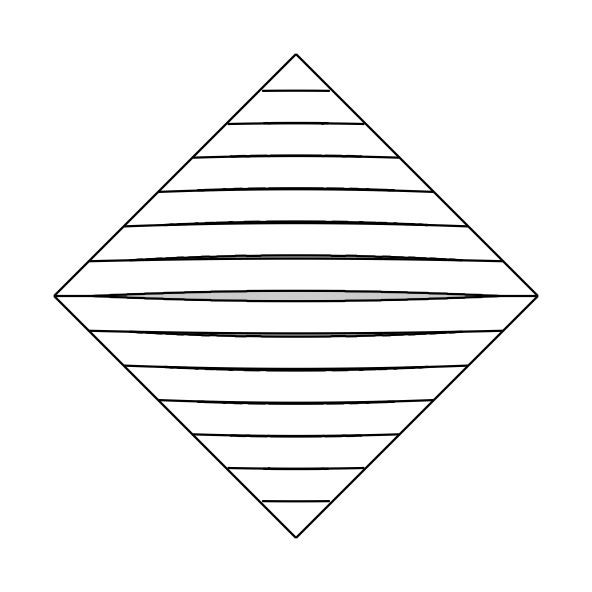

```mathematica
Show[
ListLinePlot[{ShortPPCutLineat100,ShortPNCutLineat100},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{Reverse[ShortNPCutLineat100],Reverse[ShortNNCutLineat100]},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[ShortPPOriLineat0[[293;;350]],PlotStyle->Black],
ListLinePlot[ShortNNOriLineat0[[293;;350]],PlotStyle->Black],
ListLinePlot[{ShortPPCutLineat200,ShortPPOriLineat100},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{Reverse[ShortNPCutLineat200],Reverse[ShortNPOriLineat100]},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{ShortPNCutLineat200,ShortPNOriLineat100},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{Reverse[ShortNNCutLineat200],Reverse[ShortNNOriLineat100]},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{ShortPPCutLineat300,ShortPPOriLineat200},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{Reverse[ShortNPCutLineat300],Reverse[ShortNPOriLineat200]},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{ShortPNCutLineat300,ShortPNOriLineat200},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{Reverse[ShortNNCutLineat300],Reverse[ShortNNOriLineat200]},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{ShortPPCutLineat400,ShortPPOriLineat300},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{Reverse[ShortNPCutLineat400],Reverse[ShortNPOriLineat300]},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{ShortPNCutLineat400,ShortPNOriLineat300},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{Reverse[ShortNNCutLineat400],Reverse[ShortNNOriLineat300]},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{ShortPPCutLineat500,ShortPPOriLineat400},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{Reverse[ShortNPCutLineat500],Reverse[ShortNPOriLineat400]},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{ShortPNCutLineat500,ShortPNOriLineat400},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{Reverse[ShortNNCutLineat500],Reverse[ShortNNOriLineat400]},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{ShortPPCutLineat600,ShortPPOriLineat500},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{Reverse[ShortNPCutLineat600],Reverse[ShortNPOriLineat500]},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{ShortPNCutLineat600,ShortPNOriLineat500},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{Reverse[ShortNNCutLineat600],Reverse[ShortNNOriLineat500]},Filling->{1->{2}},PlotStyle->Black],
ListLinePlot[{ShortPPOriLineat600,ShortNPOriLineat600,ShortPNOriLineat600,ShortNNOriLineat600},PlotStyle->Black],

ListLinePlot[{{{0.35,0},{0,0.75}},{{-0.35,0},{0,0.75}},{{0.35,0},{0,-0.75}},{{-0.35,0},{0,-0.75}}},PlotStyle->Black],
PlotRange-> All,Axes-> False,AspectRatio-> 1]
```

#### Piece by piece

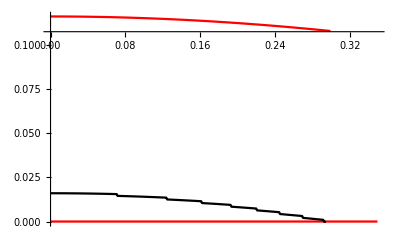

```mathematica
Show[ListLinePlot[xyvalueOri[0,0.116,100,300,1],PlotStyle->Red],ListLinePlot[xyvalueOri[0,0,0,350,1],PlotStyle->Red],ListLinePlot[xyvalue[0,0.116,0,100,300,298,1],PlotStyle->Black],PlotRange-> All]
```

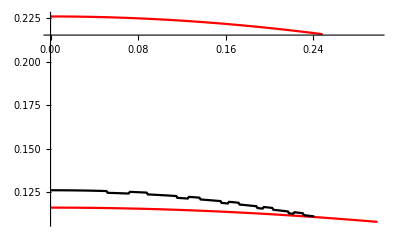

```mathematica
Show[ListLinePlot[xyvalueOri[0,0.226,200,250,1],PlotStyle->Red],ListLinePlot[xyvalueOri[0,0.116,100,300,1],PlotStyle->Red],ListLinePlot[xyvalue[0,0.226,100,200,250,242,1],PlotStyle->Black],PlotRange-> All]
```

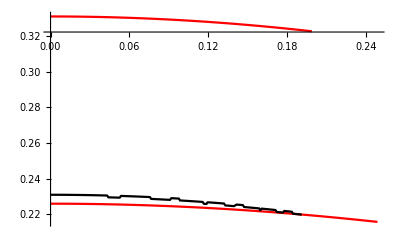

```mathematica
Show[ListLinePlot[xyvalueOri[0,0.331,300,200,1],PlotStyle->Red],ListLinePlot[xyvalueOri[0,0.226,200,250,1],PlotStyle->Red],ListLinePlot[xyvalue[0,0.331,200,300,200,187,1],PlotStyle->Black],PlotRange-> All]
```

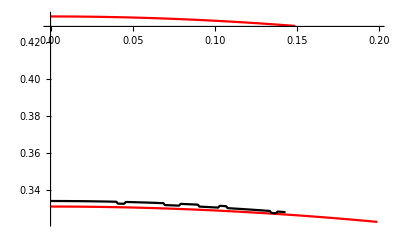

```mathematica
Show[ListLinePlot[xyvalueOri[0,0.434,400,150,1],PlotStyle->Red],ListLinePlot[xyvalueOri[0,0.331,300,200,1],PlotStyle->Red],ListLinePlot[xyvalue[0,0.434,300,400,150,134,1],PlotStyle->Black],PlotRange-> All]
```

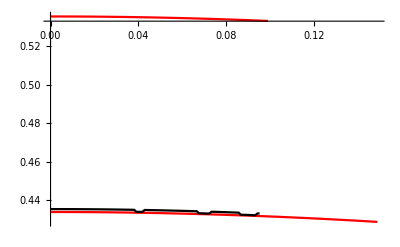

```mathematica
Show[ListLinePlot[xyvalueOri[0,0.5355,500,100,1],PlotStyle->Red],ListLinePlot[xyvalueOri[0,0.434,400,150,1],PlotStyle->Red],ListLinePlot[xyvalue[0,0.5355,400,500,100,86,1],PlotStyle->Black],PlotRange-> All]
```

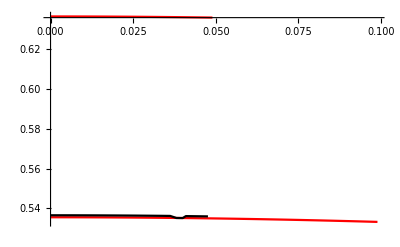

```mathematica
Show[ListLinePlot[xyvalueOri[0,0.6365,600,50,1],PlotStyle->Red],ListLinePlot[xyvalueOri[0,0.5355,500,100,1],PlotStyle->Red],ListLinePlot[xyvalue[0,0.6365,500,600,50,41,1],PlotStyle->Black],PlotRange-> All]
```

## Section 3.2

## Compute Significant Error of curvature line on Hyperbolic Paraboloid between CPU and GPU - using double for all function

### HP in GPU

```mathematica
kernelcodeHP="
#define min 0
#define max 1
#define uuu 0
#define vvv 1
#define sign1 1
#define h 0.001
#define n 1402
#define n_j 302


#define dxdu1 (tu1)
#define dxdu2 (0)
#define dxdu3 (tu2)
#define dxdv1 (0)
#define dxdv2 (tv1)
#define dxdv3 (tv2)

#define d2xdu21 (dtu1)
#define d2xdu22 (0)
#define d2xdu23 (dtu2)
#define d2xdv21 (0)
#define d2xdv22 (dtv1)
#define d2xdv23 (dtv2)
#define d2xdudv1 (0)
#define d2xdudv2 (0)
#define d2xdudv3 (0)

#define d3xdu31 (d2tu1)
#define d3xdu32 (0)
#define d3xdu33 (d2tu2)
#define d3xdv31 (0)
#define d3xdv32 (d2tv1)
#define d3xdv33 (d2tv2)
#define d3xdu2dv1 (0)
#define d3xdu2dv2 (0)
#define d3xdu2dv3 (0)
#define d3xdudv21 (0)
#define d3xdudv22 (0)
#define d3xdudv23 (0)



#define repSurNorvec SurNorvec(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,normv_C)
#define repDSurNvDu DSurNvDu(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,dnormvdu_C)
#define repDSurNvDv DSurNvDv(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,dnormvdv_C)
#define repScalarSurNor ScalarSurNor(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,Scal)
#define repcoefE coefE(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repDEDu DEDu(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repDEDv DEDv(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repcoefF coefF(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repDFDu DFDu(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repDFDv DFDv(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repcoefG coefG(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repDGDu DGDu(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repDGDv DGDv(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repcoefL coefL(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repcoefM coefM(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repcoefN coefN(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repGaussCurva GaussCurva(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repMeanCurva MeanCurva(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repMaxPrinci MaxPrinci(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repMinPrinci MinPrinci(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repPrinci Princi(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)

#define repDcoefL_2 DcoefL_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,CoeffL)
#define repDcoefM_2 DcoefM_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,CoeffM)
#define repDcoefN_2 DcoefN_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,CoeffN)
#define repDGaussCurva_2 DGaussCurva_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,GCurva)
#define repDMeanCurva_2 DMeanCurva_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,MCurva)
#define repDPrinci_2 DPrinci_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,PCurva)
#define repEta Eta(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repMiu  Miu(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDuDs DuDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDvDs DvDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDEDs DEDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDFDs DFDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDGDs DGDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDLDs DLDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDMDs DMDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDNDs DNDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDPrinciDs DPrinciDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDvDt DvDt(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDuDt DuDt(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDSurDs DSurDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,tangv)
#define repSurNor SurNor(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,Snor_C)
#define repBinormalSur BinormalSur(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,binormv_C)
#define repAlp1 Alp1(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,Alp1_C)
#define repBeta1 Beta1(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repCurvecurvature Curvecurvature(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,D2uDs2,D2vDs2,GeoCur,optimum)


#define opt1 (double xu1,double xu2,double tu1,double tu2,double dtu1,double dtu2,double xv1,double xv2,double tv1,double tv2,double dtv1,double dtv2,double normv_C[])
#define opt2 (double xu1,double xu2,double tu1,double tu2,double dtu1,double dtu2,double xv1,double xv2,double tv1,double tv2,double dtv1,double dtv2)
#define opt3 (double xu1,double xu2,double tu1,double tu2,double dtu1,double dtu2,double d2tu1,double d2tu2,double xv1,double xv2,double tv1,double tv2,double dtv1,double dtv2,double d2tv1,double d2tv2)
#define opt4 (double xu1,double xu2,double tu1,double tu2,double dtu1,double dtu2,double d2tu1,double d2tu2,double xv1,double xv2,double tv1,double tv2,double dtv1,double dtv2,double d2tv1,double d2tv2,mint optimum)
 #define opt5 (double xu1,double xu2,double tu1,double tu2,double dtu1,double dtu2,double d2tu1,double d2tu2,double xv1,double xv2,double tv1,double tv2,double dtv1,double dtv2,double d2tv1,double d2tv2,mint optimum,double tangv_C[])
#define opt6 (double xu1,double xu2,double tu1,double tu2,double dtu1,double dtu2,double d2tu1,double d2tu2,double xv1,double xv2,double tv1,double tv2,double dtv1,double dtv2,double d2tv1,double d2tv2,double dnormv_C[])
#define opt7 (double xu1,double xu2,double tu1,double tu2,double dtu1,double dtu2,double d2tu1,double d2tu2,double xv1,double xv2,double tv1,double tv2,double dtv1,double dtv2,double d2tv1,double d2tv2,double Scal[])
#define opt8 (double xu1,double xu2,double tu1,double tu2,double dtu1,double dtu2,double d2tu1,double d2tu2,double xv1,double xv2,double tv1,double tv2,double dtv1,double dtv2,double d2tv1,double d2tv2,double coeff[])
#define opt9 (double xu1,double xu2,double tu1,double tu2,double dtu1,double dtu2,double d2tu1,double d2tu2,double xv1,double xv2,double tv1,double tv2,double dtv1,double dtv2,double d2tv1,double d2tv2,mint optimum,double coeff[])
#define opt10 (double xu1,double xu2,double tu1,double tu2,double dtu1,double dtu2,double d2tu1,double d2tu2,double xv1,double xv2,double tv1,double tv2,double dtv1,double dtv2,double d2tv1,double d2tv2,mint optimum)
#define opt11 (double xu1,double xu2,double tu1,double tu2,double dtu1,double dtu2,double d2tu1,double d2tu2,double xv1,double xv2,double tv1,double tv2,double dtv1,double dtv2,double d2tv1,double d2tv2,mint optimum,double Alph_C[])
#define opt12 (double xu1,double xu2,double tu1,double tu2,double dtu1,double dtu2,double xv1,double xv2,double tv1,double tv2,double dtv1,double dtv2,double Snor_C[])
#define opt13 (double xu1,double xu2,double tu1,double tu2,double dtu1,double dtu2,double d2tu1,double d2tu2,double xv1,double xv2,double tv1,double tv2,double dtv1,double dtv2,double d2tv1,double d2tv2,mint optimum,double binormv_C[])
#define opt14 (double xu1,double xu2,double tu1,double tu2,double dtu1,double dtu2,double d2tu1,double d2tu2,double xv1,double xv2,double tv1,double tv2,double dtv1,double dtv2,double d2tv1,double d2tv2,mint optimum,double x[])




__device__ void SurNorvec opt1 
{
	normv_C[0] =dxdu2*dxdv3-dxdu3*dxdv2; 
	normv_C[1] =dxdu3*dxdv1-dxdu1*dxdv3;
	normv_C[2] =dxdu1*dxdv2-dxdu2*dxdv1; 
}
__device__ void DSurNvDu opt6
{
	dnormv_C[0] =(d2xdu22*dxdv3-d2xdu23*dxdv2)+(dxdu2*d2xdudv3-dxdu3*d2xdudv2); 
	dnormv_C[1] =(d2xdu23*dxdv1-d2xdu21*dxdv3)+(dxdu3*d2xdudv1-dxdu1*d2xdudv3);
	dnormv_C[2] =(d2xdu21*dxdv2-d2xdu22*dxdv1)+(dxdu1*d2xdudv2-dxdu2*d2xdudv1); 
}
__device__ void DSurNvDv opt6
{
	dnormv_C[0] =(d2xdudv2*dxdv3-d2xdudv3*dxdv2)+(dxdu2*d2xdv23-dxdu3*d2xdv22); 
	dnormv_C[1] =(d2xdudv3*dxdv1-d2xdudv1*dxdv3)+(dxdu3*d2xdv21-dxdu1*d2xdv23); 
	dnormv_C[2] =(d2xdudv1*dxdv2-d2xdudv2*dxdv1)+(dxdu1*d2xdv22-dxdu2*d2xdv21); 
}

__device__ void ScalarSurNor opt7
{
double ScalSNor,DScalSNorDu,DScalSNorDv;
double normv_C[3];
double dnormvdu_C[3];
double dnormvdv_C[3];

repSurNorvec;
repDSurNvDu;
repDSurNvDv;


ScalSNor = sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
DScalSNorDu = (normv_C[0]*dnormvdu_C[0]+normv_C[1]*dnormvdu_C[1]+normv_C[2]*dnormvdu_C[2])/ScalSNor;
DScalSNorDv = (normv_C[0]*dnormvdv_C[0]+normv_C[1]*dnormvdv_C[1]+normv_C[2]*dnormvdv_C[2])/ScalSNor;


Scal[0] = ScalSNor;
Scal[1] = DScalSNorDu;
Scal[2] = DScalSNorDv;
}

__device__ double coefE opt2
{
	return dxdu1*dxdu1+dxdu2*dxdu2+dxdu3*dxdu3; 
}
__device__ double DEDu opt3
{
	return 2*(dxdu1*d2xdu21+dxdu2*d2xdu22+dxdu3*d2xdu23);
}
__device__ double DEDv opt3
{
	return 2*(dxdu1*d2xdudv1+dxdu2*d2xdudv2+dxdu3*d2xdudv3);
}

 
__device__ double coefF opt2
{ 
	return (dxdu1*dxdv1+dxdu2*dxdv2+dxdu3*dxdv3); 
}
__device__ double DFDu opt3
{ 
	return dxdv1*d2xdu21+dxdv2*d2xdu22+dxdv3*d2xdu23 + dxdu1*d2xdudv1+dxdu2*d2xdudv2+dxdu3*d2xdudv3;
}
__device__ double DFDv opt3
{ 
	return dxdv1*d2xdudv1+dxdv2*d2xdudv2+dxdv3*d2xdudv3 + dxdu1*d2xdv21+dxdu2*d2xdv22+dxdu3*d2xdv23;
}

__device__ double coefG opt2
{ 
	return dxdv1*dxdv1+dxdv2*dxdv2+dxdv3*dxdv3; 
}
__device__ double DGDu opt3
{ 
	return 2*(dxdv1*d2xdudv1+dxdv2*d2xdudv2+dxdv3*d2xdudv3);
}
__device__ double DGDv opt3
{ 
	return 2*(dxdv1*d2xdv21+dxdv2*d2xdv22+dxdv3*d2xdv23);
}

__device__ double coefL opt3
{
double normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdu21+normv_C[1]*d2xdu22+normv_C[2]*d2xdu23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ double coefM opt3
{
double normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdudv1+normv_C[1]*d2xdudv2+normv_C[2]*d2xdudv3)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ double coefN opt3
{
double normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdv21+normv_C[1]*d2xdv22+normv_C[2]*d2xdv23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ double GaussCurva opt3
{
	return (repcoefL*repcoefN-pow(repcoefM,2))/(repcoefE*repcoefG-pow(repcoefF,2)); 
}
__device__ double MeanCurva opt3
{
	return 0.5*(repcoefE*repcoefN+repcoefG*repcoefL-2*repcoefF*repcoefM)/(repcoefE*repcoefG-pow(repcoefF,2));
}
__device__ double MaxPrinci opt3
{
	return repMeanCurva+sqrt(pow(repMeanCurva,2)-repGaussCurva); 
}

__device__ double MinPrinci opt3
{
	return repMeanCurva-sqrt(pow(repMeanCurva,2)-repGaussCurva); 
}
__device__ double Princi opt4
{ 	
	if(optimum==max) 
	{return repMaxPrinci;} 
	else if(optimum==min)
	{return repMinPrinci;}
	else
	{return 0;}
}
__device__ void DcoefL_2 opt8
{

double CoeL,DCoeLDu,DCoeLDv;
double normv_C[3];
double dnormvdu_C[3];
double dnormvdv_C[3];
double Scal[3];

repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repScalarSurNor;

CoeL = (normv_C[0]*d2xdu21+normv_C[1]*d2xdu22+normv_C[2]*d2xdu23)/Scal[0];
DCoeLDu = ((dnormvdu_C[0]*d2xdu21+dnormvdu_C[1]*d2xdu22+dnormvdu_C[2]*d2xdu23)+(normv_C[0]*d3xdu31+normv_C[1]*d3xdu32+normv_C[2]*d3xdu33)-Scal[1]*CoeL)/Scal[0];
DCoeLDv = ((dnormvdv_C[0]*d2xdu21+dnormvdv_C[1]*d2xdu22+dnormvdv_C[2]*d2xdu23)+(normv_C[0]*d3xdu2dv1+normv_C[1]*d3xdu2dv2+normv_C[2]*d3xdu2dv3)-Scal[2]*CoeL)/Scal[0];

coeff[0] = CoeL;
coeff[1] = DCoeLDu;
coeff[2] = DCoeLDv;

}
__device__ void DcoefM_2 opt8
{
double CoeM,DCoeMDu,DCoeMDv;
double normv_C[3];
double dnormvdu_C[3];
double dnormvdv_C[3];
double Scal[3];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repScalarSurNor;

CoeM = (normv_C[0]*d2xdudv1+normv_C[1]*d2xdudv2+normv_C[2]*d2xdudv3)/Scal[0];
DCoeMDu = ((dnormvdu_C[0]*d2xdudv1+dnormvdu_C[1]*d2xdudv2+dnormvdu_C[2]*d2xdudv3)+(normv_C[0]*d3xdu2dv1+normv_C[1]*d3xdu2dv2+normv_C[2]*d3xdu2dv3)-Scal[1]*CoeM)/Scal[0];
DCoeMDv = ((dnormvdv_C[0]*d2xdudv1+dnormvdv_C[1]*d2xdudv2+dnormvdv_C[2]*d2xdudv3)+(normv_C[0]*d3xdudv21+normv_C[1]*d3xdudv22+normv_C[2]*d3xdudv23)-Scal[2]*CoeM)/Scal[0];


coeff[0] = CoeM;
coeff[1] = DCoeMDu;
coeff[2] = DCoeMDv;
}
__device__ void DcoefN_2 opt8
{
double CoeN,DCoeNDu,DCoeNDv;
double normv_C[3];
double dnormvdu_C[3];
double dnormvdv_C[3];
double Scal[3];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repScalarSurNor;

CoeN = (normv_C[0]*d2xdv21+normv_C[1]*d2xdv22+normv_C[2]*d2xdv23)/Scal[0];
DCoeNDu = ((dnormvdu_C[0]*d2xdv21+dnormvdu_C[1]*d2xdv22+dnormvdu_C[2]*d2xdv23)+(normv_C[0]*d3xdudv21+normv_C[1]*d3xdudv22+normv_C[2]*d3xdudv23)-Scal[1]*CoeN)/Scal[0];
DCoeNDv = ((dnormvdv_C[0]*d2xdv21+dnormvdv_C[1]*d2xdv22+dnormvdv_C[2]*d2xdv23)+(normv_C[0]*d3xdv31+normv_C[1]*d3xdv32+normv_C[2]*d3xdv33)-Scal[2]*CoeN)/Scal[0];

coeff[0] = CoeN;
coeff[1] = DCoeNDu;
coeff[2] = DCoeNDv;

}
__device__ void DGaussCurva_2 opt8 
{
double GCurv,DGCurvDu,DGCurvDv;
double CoeffL[3];
double CoeffM[3];
double CoeffN[3];
repDcoefL_2;
repDcoefM_2;
repDcoefN_2;

GCurv= (CoeffL[0]*CoeffN[0]-pow(CoeffM[0],2))/(repcoefE*repcoefG-pow(repcoefF,2));
DGCurvDu = ((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*CoeffL[1]-2*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
DGCurvDv =((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*CoeffL[2]-2*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));


coeff[0] = GCurv;
coeff[1] = DGCurvDu;
coeff[2] = DGCurvDv;

}
__device__ void DMeanCurva_2 opt8
{
double MCurv,DMCurvDu,DMCurvDv;
double CoeffL[3];
double CoeffM[3];
double CoeffN[3];
repDcoefL_2;
repDcoefM_2;
repDcoefN_2;

MCurv = 0.5*(repcoefE*CoeffN[0]+repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0])/(repcoefE*repcoefG-pow(repcoefF,2));
DMCurvDu = 0.5*(-(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*repDEDu-2*CoeffM[0]*repDFDu+CoeffL[0]*repDGDu+repcoefG*CoeffL[1]-2*repcoefF*CoeffM[1]+repcoefE*CoeffN[1]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
DMCurvDv = 0.5*(-(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*repDEDv-2*CoeffM[0]*repDFDv+CoeffL[0]*repDGDv+repcoefG*CoeffL[2]-2*repcoefF*CoeffM[2]+repcoefE*CoeffN[2]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));



coeff[0] = MCurv;
coeff[1] = DMCurvDu;
coeff[2] = DMCurvDv;
}
__device__ void DPrinci_2 opt9
{
double Princip,DPrincipDu,DPrincipDv;
double GCurva[3];
double MCurva[3];
repDGaussCurva_2;
repDMeanCurva_2;

if(optimum==max) 
{Princip = MCurva[0]+sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]+(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]+(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));

}
else if(optimum==min)
{Princip = MCurva[0]-sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]-(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]-(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));

}
else
{Princip = 0;
DPrincipDu = 0;
DPrincipDv = 0;
}

coeff[0] = Princip;
coeff[1] = DPrincipDu;
coeff[2] = DPrincipDv;

}

__device__ double Eta opt4
{
	return sign1/sqrt(repcoefE*pow(repcoefM-repPrinci*repcoefF,2)-2*repcoefF*(repcoefM-repPrinci*repcoefF)*(repcoefL-repPrinci*repcoefE)+repcoefG*pow(repcoefL-repPrinci*repcoefE,2));
}
__device__ double Miu opt4
{
	return sign1/sqrt(repcoefE*pow(repcoefN-repPrinci*repcoefG,2)-2*repcoefF*(repcoefM-repPrinci*repcoefF)*(repcoefN-repPrinci*repcoefG)+repcoefG*pow(repcoefM-repPrinci*repcoefF,2));
}
__device__ double DuDs opt4
{ 
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return repEta*(repcoefM-repPrinci*repcoefF);}
else
	{return repMiu*(repcoefN-repPrinci*repcoefG);}
}
__device__ double DvDs opt4
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return -repEta*(repcoefL-repPrinci*repcoefE);}
else
	{return -repMiu*(repcoefM-repPrinci*repcoefF);}
}
__device__ double DEDs opt4
{
	return repDEDu*repDuDs+repDEDv*repDvDs;
}
__device__ double DFDs opt4
{
	return repDFDu*repDuDs+repDFDv*repDvDs;
}
__device__ double DGDs opt4
{
	return repDGDu*repDuDs+repDGDv*repDvDs;
}
__device__ double DLDs opt10
{
double CoeffL[3];
repDcoefL_2;

	return CoeffL[1]*repDuDs+CoeffL[2]*repDvDs;
}
__device__ double DMDs opt10
{
double CoeffM[3];
repDcoefM_2;

	return CoeffM[1]*repDuDs+CoeffM[2]*repDvDs;
}
__device__ double DNDs opt10
{
double CoeffN[3];
repDcoefN_2;

	return CoeffN[1]*repDuDs+CoeffN[2]*repDvDs;
}
__device__ double DPrinciDs opt10
{
double PCurva[3];
repDPrinci_2;

	return PCurva[1]*repDuDs+PCurva[2]*repDvDs;
}
__device__ double DuDt opt4
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return (repcoefM-repPrinci*repcoefF);}
else
	{return (repcoefN-repPrinci*repcoefG);}
}
__device__ double DvDt opt4
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return (repcoefL-repPrinci*repcoefE);}
else
	{return (repcoefM-repPrinci*repcoefF);}
}
__device__ void DSurDs opt5
{
	tangv_C[0] =dxdu1*repDuDs+dxdv1*repDvDs;
	tangv_C[1] =dxdu2*repDuDs+dxdv2*repDvDs;
	tangv_C[2] =dxdu3*repDuDs+dxdv3*repDvDs;
}

__device__ void Alp1 opt11
{
	Alph_C[0]=(d2xdu21*pow(repDuDs,2)+2*d2xdudv1*repDuDs*repDvDs+d2xdv21*pow(repDvDs,2));
	Alph_C[1]=(d2xdu22*pow(repDuDs,2)+2*d2xdudv2*repDuDs*repDvDs+d2xdv22*pow(repDvDs,2));
	Alph_C[2]=(d2xdu23*pow(repDuDs,2)+2*d2xdudv3*repDuDs*repDvDs+d2xdv23*pow(repDvDs,2));
}
__device__ void SurNor opt12 
{
	double normv_C[3];
	repSurNorvec;
	Snor_C[0] =normv_C[0]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]); 
	Snor_C[1] =normv_C[1]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
	Snor_C[2] =normv_C[2]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]); 
}

__device__ void BinormalSur opt13
{
	double Snor_C[3];
	double tangv[3];
	repSurNor;
	repDSurDs;

	binormv_C[0] =Snor_C[1]*tangv[2] -Snor_C[2]*tangv[1];
	binormv_C[1] =Snor_C[2]*tangv[0] -Snor_C[0]*tangv[2];
	binormv_C[2] =Snor_C[0]*tangv[1] -Snor_C[1]*tangv[0];
}
__device__ double Beta1 opt10
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return (-(repDLDs-repDPrinciDs*repcoefE-repPrinci*repDEDs)*repDuDs-(repDMDs-repDPrinciDs*repcoefF-repPrinci*repDFDs)*repDvDs);}
else
	{return (-(repDMDs-repDPrinciDs*repcoefF-repPrinci*repDFDs)*repDuDs-(repDNDs-repDPrinciDs*repcoefG-repPrinci*repDGDs)*repDvDs);}
}

__device__ void LUDecomposition3x3 opt14
{
	int rc=3;
	double binormv_C[3];
	double Alp1_C[3];
	repBinormalSur;
	repAlp1;
	double matrixA[3][3]={
	{repcoefE,repcoefF,-(binormv_C[0]*dxdu1+binormv_C[1]*dxdu2+binormv_C[2]*dxdu3)},
	{repcoefF,repcoefG,-(binormv_C[0]*dxdv1+binormv_C[1]*dxdv2+binormv_C[2]*dxdv3)},
	{repDvDt,repDuDt,0}};

	double matrixB[3]={-(Alp1_C[0]*dxdu1+Alp1_C[1]*dxdu2+Alp1_C[2]*dxdu3),-(Alp1_C[0]*dxdv1+Alp1_C[1]*dxdv2+Alp1_C[2]*dxdv3),repBeta1};
	double Lower[3][3];
	double Upper[3][3];
	double y[3];
	double sum;
	for(int ii=0; ii<rc; ii++)
			{
				for(int jj=0; jj<rc; jj++)
				{
					sum = 0;
					if(ii==jj)
					{
					Lower[ii][jj]=1;
					for (int kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else if(ii < jj) 
					{
					Lower[ii][jj]=0;
					for (int kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else 
					{
					Upper[ii][jj]=0;
					for (int kk = 0; kk < jj; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Lower[ii][jj] =(matrixA[ii][jj] - sum)/Upper[jj][jj];
					}
				}
			}
	for (int ii = 0; ii < rc; ii++)
	{
		sum = 0;
		for (int jj = 0; jj < ii; jj++)
			{sum += Lower[ii][jj] * y[jj];}
		y[ii] = matrixB[ii] - sum;
	}
	for (int ii = rc - 1; ii >= 0; ii--)
	{
		sum = 0;
		for (int jj = ii + 1; jj < rc; jj++)
			{sum += Upper[ii][jj] * x[jj];}
		x[ii] = (y[ii] - sum)/Upper[ii][ii];
	}
}


__device__ double RK4_Init(double x1, double t1, double SSize) 
  
{
double k1,k2,k3,k4;

k1=SSize*x1;
k2=SSize*(x1+0.5*SSize*t1);
k3=SSize*(x1+0.5*SSize*t1);
k4=SSize*(x1+SSize*t1);

return (1.0/6.0)*(k1+2*k2+2*k3+k4);
}

__device__ double RK4_Init2(double x1, double t1, double SSize) 
  
{
double k1,k2,k3,k4;

k1=SSize*x1;
k2=SSize*(x1+0.5*SSize*t1);
k3=SSize*(x1+0.5*SSize*t1);
k4=SSize*(x1+SSize*t1);

return (1.0/6.0)*(k1+2*k2+2*k3+k4);
}

__device__ void RK4_func( double xu1, double xu2, double tu1, double tu2, double dtu1, double dtu2, double d2tu1, double d2tu2, double xv1, double xv2, double tv1, double tv2, double dtv1, double dtv2, double d2tv1, double d2tv2, mint optimum, double& increment_u, double& increment_v) 
  
{

double ku1,ku2,ku3,ku4;
double kv1,kv2,kv3,kv4;
double newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2;
double newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2;


ku1=h*DuDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum);
kv1=h*DvDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum);

newxu1=xu1+0.5*ku1*tu1;
newxu2=xu2+0.5*ku1*tu2;
newtu1=tu1+0.5*ku1*dtu1;
newtu2=tu2+0.5*ku1*dtu2;
newdtu1=0;
newdtu2=2;
newxv1=xv1+0.5*kv1*tv1;
newxv2=xv2+0.5*kv1*tv2;
newtv1=tv1+0.5*kv1*dtv1;
newtv2=tv2+0.5*kv1*dtv2;
newdtv1=0;
newdtv2=-2;
ku2=h*DuDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,d2tu1,d2tu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,d2tv1,d2tv2,optimum);
kv2=h*DvDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,d2tu1,d2tu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,d2tv1,d2tv2,optimum);

newxu1=xu1+0.5*ku2*tu1;
newxu2=xu2+0.5*ku2*tu2;
newtu1=tu1+0.5*ku2*dtu1;
newtu2=tu2+0.5*ku2*dtu2;
newdtu1=0;
newdtu2=2;
newxv1=xv1+0.5*kv2*tv1;
newxv2=xv2+0.5*kv2*tv2;
newtv1=tv1+0.5*kv2*dtv1;
newtv2=tv2+0.5*kv2*dtv2;
newdtv1=0;
newdtv2=-2;

ku3=h*DuDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,d2tu1,d2tu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,d2tv1,d2tv2,optimum);
kv3=h*DvDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,d2tu1,d2tu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,d2tv1,d2tv2,optimum);

newxu1=xu1+ku3*tu1;
newxu2=xu2+ku3*tu2;
newtu1=tu1+ku3*dtu1;
newtu2=tu2+ku3*dtu2;
newdtu1=0;
newdtu2=2;
newxv1=xv1+kv3*tv1;
newxv2=xv2+kv3*tv2;
newtv1=tv1+kv3*dtv1;
newtv2=tv2+kv3*dtv2;
newdtv1=0;
newdtv2=-2;

ku4=h*DuDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,d2tu1,d2tu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,d2tv1,d2tv2,optimum);
kv4=h*DvDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,d2tu1,d2tu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,d2tv1,d2tv2,optimum);

increment_u=(1.0/6.0)*(ku1+2*ku2+2*ku3+ku4);
increment_v=(1.0/6.0)*(kv1+2*kv2+2*kv3+kv4);

}

__device__ void ReturnGeoCur( int k, double x[], double y[], double z[], double GeoCur[], mint optimum)  
{
double iniSSize_u,iniSSize_v,SSize_u,SSize_v;

double xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2;
double xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2;
double u_s, dummyu_s;
double v_s, dummyv_s;
double coef[3];

u_s=0;
v_s=0;
dummyu_s=u_s;
dummyv_s=v_s;
xu1=0;
xu2=0;
tu1=1;
tu2=0;
dtu1=0;
dtu2=2;
d2tu1=0;
d2tu2=0;
xv1=0;
xv2=0;
tv1=1;
tv2=0;
dtv1=0;
dtv2=-2;
d2tv1=0;
d2tv2=0;

if(optimum==min)
{
	for(int i=1;i<=k;i++)
	{
		RK4_func(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,max,SSize_u,SSize_v);
		u_s+=SSize_u;		
		v_s+=SSize_v;
		dummyu_s=u_s;
		dummyv_s=v_s;
		xu1+=RK4_Init(tu1,dtu1,SSize_u);
		xu2+=RK4_Init(tu2,dtu2,SSize_u);
		tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
		tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
		dtu1=0;
		dtu2=2;
		d2tu1=0;
		d2tu2=0;
		xv1+=RK4_Init(tv1,dtv1,SSize_v);
		xv2+=RK4_Init(tv2,dtv2,SSize_v);
		tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
		tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
		dtv1=0;
		dtv2=-2;
		d2tv1=0;
		d2tv2=0;
	}

	x[0]=xu1;
	y[0]=xv1;
	z[0]=xu2+xv2;
	LUDecomposition3x3(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,coef);
	GeoCur[0]=coef[2];

	for(int j=1;j<n;j++)
	{
		RK4_func(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,SSize_u,SSize_v);
		u_s+=SSize_u;		
		v_s+=SSize_v;
		dummyu_s=u_s;
		dummyv_s=v_s;
		xu1+=RK4_Init(tu1,dtu1,SSize_u);
		xu2+=RK4_Init(tu2,dtu2,SSize_u);
		tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
		tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
		dtu1=0;
		dtu2=2;
		d2tu1=0;
		d2tu2=0;
	
		xv1+=RK4_Init(tv1,dtv1,SSize_v);
		xv2+=RK4_Init(tv2,dtv2,SSize_v);
		tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
		tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
		dtv1=0;
		dtv2=-2;
		d2tv1=0;
		d2tv2=0;

		x[j]=xu1;
		y[j]=xv1;
		z[j]=xu2+xv2;
		LUDecomposition3x3(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,coef);
		GeoCur[j]=coef[2];

	}

}
else if(optimum==max) 
{
	for(int i=1;i<=k;i++)
	{

		RK4_func(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,min,SSize_u,SSize_v);
		u_s+=SSize_u;		
		v_s+=SSize_v;
		dummyu_s=u_s;
		dummyv_s=v_s;
		xu1+=RK4_Init(tu1,dtu1,SSize_u);
		xu2+=RK4_Init(tu2,dtu2,SSize_u);
		tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
		tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
		dtu1=0;
		dtu2=2;
		d2tu1=0;
		d2tu2=0;
		xv1+=RK4_Init(tv1,dtv1,SSize_v);
		xv2+=RK4_Init(tv2,dtv2,SSize_v);
		tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
		tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
		dtv1=0;
		dtv2=-2;
		d2tv1=0;
		d2tv2=0;
	}

	x[0]=xu1;
	y[0]=xv1;
	z[0]=xu2+xv2;
	LUDecomposition3x3(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,coef);
	GeoCur[0]=coef[2];

	for(int j=1;j<n;j++)
	{
		RK4_func(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,SSize_u,SSize_v);
		u_s+=SSize_u;		
		v_s+=SSize_v;
		dummyu_s=u_s;
		dummyv_s=v_s;
		xu1+=RK4_Init(tu1,dtu1,SSize_u);
		xu2+=RK4_Init(tu2,dtu2,SSize_u);
		tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
		tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
		dtu1=0;
		dtu2=2;
		d2tu1=0;
		d2tu2=0;
	
		xv1+=RK4_Init(tv1,dtv1,SSize_v);
		xv2+=RK4_Init(tv2,dtv2,SSize_v);
		tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
		tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
		dtv1=0;
		dtv2=-2;
		d2tv1=0;
		d2tv2=0;

		x[j]=xu1;
		y[j]=xv1;
		z[j]=xu2+xv2;
		LUDecomposition3x3(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,coef);
		GeoCur[j]=coef[2];

	}



}

}




__global__ void fun( double * xvalue, double * yvalue, double * zvalue, double * Geovalue, mint init_s, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
double x1[n], y1[n], z1[n];
double GeoCur1[n];


ReturnGeoCur( init_s, x1, y1, z1, GeoCur1, optimum);

if( index < ListSize)
{
	xvalue[index]= x1[index];
	yvalue[index]= y1[index];
	zvalue[index]= z1[index];
	Geovalue[index]= GeoCur1[index];
}

}


";
```

```mathematica
Needs["CUDALink`"]
```

```mathematica
AbsoluteTiming[funcLoCHP1=CUDAFunctionLoad[kernelcodeHP,"fun",{{"Double",_,"Output"},{"Double",_,"Output"},{"Double",_,"Output"},{"Double",_,"Output"},_Integer,_Integer,_Integer},160]]
```

{75.1258,CUDAFunction[<>,fun,{{Double,_,Output},{Double,_,Output},{Double,_,Output},{Double,_,Output},Integer64,Integer64,Integer64}]}

```mathematica
GeoCur[v_,nn_,optimum_]:=Flatten[
bufferLoCHP61=CUDAMemoryAllocate["Double",nn];
bufferLoCHP62=CUDAMemoryAllocate["Double",nn];
bufferLoCHP63=CUDAMemoryAllocate["Double",nn];
bufferLoCHP64=CUDAMemoryAllocate["Double",nn];
resHP6=AbsoluteTiming[funcLoCHP1[bufferLoCHP61,bufferLoCHP62,bufferLoCHP63,bufferLoCHP64,v,optimum,nn]];
CUDAMemoryGet[bufferLoCHP64],0];
```

```mathematica
xyzvalue[v_,nn_,optimum_]:=Flatten[
bufferLoCHP11=CUDAMemoryAllocate["Double",nn];
bufferLoCHP12=CUDAMemoryAllocate["Double",nn];
bufferLoCHP13=CUDAMemoryAllocate["Double",nn];
bufferLoCHP14=CUDAMemoryAllocate["Double",nn];
resHP=AbsoluteTiming[funcLoCHP1[bufferLoCHP11,bufferLoCHP12,bufferLoCHP13,bufferLoCHP14,v,optimum,nn]];
Transpose[{CUDAMemoryGet[bufferLoCHP11],CUDAMemoryGet[bufferLoCHP12],CUDAMemoryGet[bufferLoCHP13]}],0];
```

### HP in CPU

```mathematica
Surf[u_,v_][s_]:={u[s],v[s],u[s]^2-v[s]^2};
DuSurf[u_,v_][s_]:={1,0,2 u[s]};
DvSurf[u_,v_][s_]:={0,1,-2 v[s]};
Du2Surf[u_,v_][s_]:={0,0,2};
Dv2Surf[u_,v_][s_]:={0,0,-2};
DuDvSurf[u_,v_][s_]:={0,0,0};
CrossN[u_,v_][s_]:=Cross[DuSurf[u,v][s],DvSurf[u,v][s]];
ScalarN[u_,v_][s_]:=Sqrt[CrossN[u,v][s].CrossN[u,v][s]];
NormalSurf[u_,v_][s_]:=CrossN[u,v][s]/ScalarN[u,v][s];
SurfE[u_,v_][s_]:=DuSurf[u,v][s].DuSurf[u,v][s];
SurfF[u_,v_][s_]:=DuSurf[u,v][s].DvSurf[u,v][s];
SurfG[u_,v_][s_]:=DvSurf[u,v][s].DvSurf[u,v][s];
SurfL[u_,v_][s_]:=Du2Surf[u,v][s].NormalSurf[u,v][s];
SurfM[u_,v_][s_]:=DuDvSurf[u,v][s].NormalSurf[u,v][s];
SurfN[u_,v_][s_]:=Dv2Surf[u,v][s].NormalSurf[u,v][s];
GaussCurva[u_,v_][s_]:=(SurfL[u,v][s] SurfN[u,v][s]-SurfM[u,v][s]^2)/(SurfE[u,v][s] SurfG[u,v][s]-SurfF[u,v][s]^2);
MeanCurva[u_,v_][s_]:=1/2 (SurfE[u,v][s] SurfN[u,v][s]+SurfG[u,v][s] SurfL[u,v][s]-2 SurfF[u,v][s] SurfM[u,v][s])/(SurfE[u,v][s] SurfG[u,v][s]-SurfF[u,v][s]^2);
MaxPrinci[u_,v_][s_]:=MeanCurva[u,v][s]+Sqrt[MeanCurva[u,v][s]^2-GaussCurva[u,v][s]];
MinPrinci[u_,v_][s_]:=MeanCurva[u,v][s]-Sqrt[MeanCurva[u,v][s]^2-GaussCurva[u,v][s]];
Princi[a_,u_,v_][s_]:=Piecewise[{{MaxPrinci[u,v][s],a=== max},{MinPrinci[u,v][s],a===min}}];

Etaη[a_,u_,v_][s_]:=1/Sqrt[SurfE[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])^2-2 SurfF[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]) (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])+SurfG[u,v][s] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])^2];
Miuμ[a_,u_,v_][s_]:=1/Sqrt[SurfE[u,v][s] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])^2-2 SurfF[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]) (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])+SurfG[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])^2];

DuDs[a_,u_,v_][s_]:=Piecewise[{{Etaη[a,u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}},Miuμ[a,u,v][s] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])]
DvDs[a_,u_,v_][s_]:=Piecewise[{{-Etaη[a,u,v][s] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}},-Miuμ[a,u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])]

d1uds1[a_,b_,c_]:=DuDs[a,u,v][s]/.{u[s]->b,v[s]->c}
d1vds1[a_,b_,c_]:=DvDs[a,u,v][s]/.{u[s]->b,v[s]->c}

DEDs[u_,v_][s_]:=D[SurfE[u,v][s],s]
DFDs[u_,v_][s_]:=D[SurfF[u,v][s],s]
DGDs[u_,v_][s_]:=D[SurfG[u,v][s],s]
DLDs[u_,v_][s_]:=D[SurfL[u,v][s],s]
DMDs[u_,v_][s_]:=D[SurfM[u,v][s],s]
DNDs[u_,v_][s_]:=D[SurfN[u,v][s],s]
DkpDs[a_,u_,v_][s_]:=D[Princi[a,u,v][s],s]
D2EDs2[u_,v_][s_]:=D[SurfE[u,v][s],{s,2}]
D2FDs2[u_,v_][s_]:=D[SurfF[u,v][s],{s,2}]
D2GDs2[u_,v_][s_]:=D[SurfG[u,v][s],{s,2}]
D2LDs2[u_,v_][s_]:=D[SurfL[u,v][s],{s,2}]
D2MDs2[u_,v_][s_]:=D[SurfM[u,v][s],{s,2}]
D2NDs2[u_,v_][s_]:=D[SurfN[u,v][s],{s,2}]
D2kpDs2[a_,u_,v_][s_]:=D[Princi[a,u,v][s],{s,2}]
DuDt[a_,u_,v_][s_]:=Piecewise[{{(SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}},(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])];
DvDt[a_,u_,v_][s_]:=Piecewise[{{(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}}, (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])];
BinormalSurf[u_,v_][s_]:=Cross[NormalSurf[u,v][s],(DuSurf[u,v][s] u'[s]+DvSurf[u,v][s] v'[s])];

Alp1[a_,u_,v_][s_]:=Du2Surf[u,v][s] (u'[s])^2+2 DuDvSurf[u,v][s] u'[s] v'[s]+Dv2Surf[u,v][s] (v'[s])^2;
Beta1[a_,u_,v_][s_]:=Piecewise[{{-(DLDs[u,v][s]-DkpDs[a,u,v][s] SurfE[u,v][s]-Princi[a,u,v][s] DEDs[u,v][s]) u'[s]-(DMDs[u,v][s]-DkpDs[a,u,v][s] SurfF[u,v][s]-Princi[a,u,v][s] DFDs[u,v][s]) v'[s],Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}}, -(DMDs[u,v][s]-DkpDs[a,u,v][s] SurfF[u,v][s]-Princi[a,u,v][s] DFDs[u,v][s]) u'[s]-(DNDs[u,v][s]-DkpDs[a,u,v][s] SurfG[u,v][s]-Princi[a,u,v][s] DGDs[u,v][s]) v'[s]];
Matris[a_,u_,v_][s_]:={{SurfE[u,v][s],SurfF[u,v][s],-BinormalSurf[u,v][s].DuSurf[u,v][s]},
{SurfF[u,v][s],SurfG[u,v][s],-BinormalSurf[u,v][s].DvSurf[u,v][s]},
{DvDt[a,u,v][s],DuDt[a,u,v][s],0}}
MatricR2[a_,u_,v_][s_]:={-Alp1[a,u,v][s].DuSurf[u,v][s],
-Alp1[a,u,v][s].DvSurf[u,v][s],
Beta1[a,u,v][s]}

InverResult[a_,b_,c_]:=N[(Inverse[Matris[a,u,v][s]/.{u'[s]->d1uds1[a,b,c],v'[s]->d1vds1[a,b,c],u[s]->b,v[s]->c}]).(MatricR2[a,u,v][s]/.{u'[s]->d1uds1[a,b,c],v'[s]->d1vds1[a,b,c],u[s]->b,v[s]->c})]
D2uDs2[a_,b_,c_]:=InverResult[a,b,c][[1]]
D2vDs2[a_,b_,c_]:=InverResult[a,b,c][[2]]
GeoCur[a_,b_,c_]:=InverResult[a,b,c][[3]]

Princi1[a_,b_,c_]:=Piecewise[{{MaxPrinci[u,v][s],a=== max},{MinPrinci[u,v][s],a===min}}]/.{u[s]->b,v[s]->c};
Curofacurve[a_,b_,c_]:=Sqrt[Princi1[a,b,c]^2+GeoCur[a,b,c]^2]
tangent1[a_,b_,c_]:=(DuSurf[u,v][s] u'[s]+DvSurf[u,v][s] v'[s])/.{u''[s]->D2uDs2[a,b,c],v''[s]->D2vDs2[a,b,c],u'[s]->d1uds1[a,b,c],v'[s]->d1vds1[a,b,c],u[s]->b,v[s]->c}
dtangentds1[a_,b_,c_]:=D[(DuSurf[u,v][s] u'[s]+DvSurf[u,v][s] v'[s]),s]/.{u''[s]->D2uDs2[a,b,c],v''[s]->D2vDs2[a,b,c],u'[s]->d1uds1[a,b,c],v'[s]->d1vds1[a,b,c],u[s]->b,v[s]->c}
normal1[a_,b_,c_]:=dtangentds1[a,b,c]/Sqrt[dtangentds1[a,b,c].dtangentds1[a,b,c]]
binormal1[a_,b_,c_]:=Cross[tangent1[a,b,c],normal1[a,b,c]]


tangent[u_,v_][s_]:=(DuSurf[u,v][s] u'[s]+DvSurf[u,v][s] v'[s]);
dtangentds[u_,v_][s_]:=D[(DuSurf[u,v][s] u'[s]+DvSurf[u,v][s] v'[s]),s];
curvature[u_,v_][s_]:=Sqrt[dtangentds[u,v][s].dtangentds[u,v][s]];
normal[u_,v_][s_]:=dtangentds[u,v][s]/curvature[u,v][s];
binormal[u_,v_][s_]:=Cross[tangent[u,v][s],normal[u,v][s]];

alpha2[u_,v_][s_]:=D[Surf[u,v][s],{u[s],3}]* u'[s]^3+3 (D[Surf[u,v][s],{u[s],2},v[s]] v'[s] u'[s]^2+D[Surf[u,v][s],{v[s],2},u[s]] u'[s] v'[s]^2)+D[Surf[u,v][s],{v[s],3}] v'[s]^3+3 (D[Surf[u,v][s],{u[s],2}] u'[s] u''[s]+D[Surf[u,v][s],u[s],v[s]] (v'[s] u''[s]+u'[s] v''[s])+D[Surf[u,v][s],{v[s],2}] v'[s] v''[s])
beta2[a_,u_,v_][s_]:=Piecewise[{{-(2 (DLDs[u,v][s]-DkpDs[a,u,v][s] SurfE[u,v][s]-Princi[a,u,v][s] DEDs[u,v][s]) u''[s]+2 (DMDs[u,v][s]-DkpDs[a,u,v][s] SurfF[u,v][s]-Princi[a,u,v][s] DFDs[u,v][s]) v''[s]+(D2LDs2[u,v][s]-D2kpDs2[a,u,v][s] SurfE[u,v][s]-2 DkpDs[a,u,v][s] DEDs[u,v][s]-Princi[a,u,v][s] D2EDs2[u,v][s]) u'[s]+(D2MDs2[u,v][s]-D2kpDs2[a,u,v][s] SurfF[u,v][s]-2 DkpDs[a,u,v][s] DFDs[u,v][s]-Princi[a,u,v][s] D2FDs2[u,v][s]) v'[s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}}, -(2 (DMDs[u,v][s]-DkpDs[a,u,v][s] SurfF[u,v][s]-Princi[a,u,v][s] DFDs[u,v][s]) u''[s]+2 (DNDs[u,v][s]-DkpDs[a,u,v][s] SurfG[u,v][s]-Princi[a,u,v][s] DGDs[u,v][s]) v''[s]+(D2MDs2[u,v][s]-D2kpDs2[a,u,v][s] SurfF[u,v][s]-2DkpDs[a,u,v][s] DFDs[u,v][s]-Princi[a,u,v][s] D2FDs2[u,v][s]) u'[s]+(D2NDs2[u,v][s]-D2kpDs2[a,u,v][s] SurfG[u,v][s]-2 DkpDs[a,u,v][s] DGDs[u,v][s]-Princi[a,u,v][s] D2GDs2[u,v][s]) v'[s])]


MatrisTor[a_,u_,v_][s_]:={
{SurfE[u,v][s],SurfF[u,v][s],-normal[u,v][s].DuSurf[u,v][s],-curvature[u,v][s] (binormal[u,v][s].DuSurf[u,v][s])},

{SurfF[u,v][s],SurfG[u,v][s],-normal[u,v][s].DvSurf[u,v][s],-curvature[u,v][s] (binormal[u,v][s].DvSurf[u,v][s])},

{normal[u,v][s].DuSurf[u,v][s],normal[u,v][s].DvSurf[u,v][s],-1,0},

{DvDt[a,u,v][s],DuDt[a,u,v][s],0,0}
}
MatricTorR2[a_,u_,v_][s_]:={
-alpha2[u,v][s] .DuSurf[u,v][s]-curvature[u,v][s]^2 tangent[u,v][s].DuSurf[u,v][s],
-alpha2[u,v][s] .DvSurf[u,v][s]-curvature[u,v][s]^2 tangent[u,v][s].DvSurf[u,v][s],
-alpha2[u,v][s].normal[u,v][s],
beta2[a,u,v][s]
}

InverResultTor[a_,b_,c_]:=N[(Inverse[MatrisTor[a,u,v][s]/.{u''[s]->D2uDs2[a,b,c],v''[s]->D2vDs2[a,b,c],u'[s]->d1uds1[a,b,c],v'[s]->d1vds1[a,b,c],u[s]->b,v[s]->c}]).(MatricTorR2[a,u,v][s]/.{u''[s]->D2uDs2[a,b,c],v''[s]->D2vDs2[a,b,c],u'[s]->d1uds1[a,b,c],v'[s]->d1vds1[a,b,c],u[s]->b,v[s]->c})]
ClassicalRK4bval={{1/2},{0,1/2},{0,0,1}};
ClassicalRK4cval={1/6,1/3,1/3,1/6};
ClassicalRK4aval ={1/2,1/2,1};
ClassicalRK4Coefficients[4,p_]:=N[{ClassicalRK4bval,ClassicalRK4cval,ClassicalRK4aval },p];


DPbval={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},
{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DPcval={35/384,0,500/1113,125/192,-2187/6784,11/84, 0};
DPaval = {1/5,3/10,4/5,8/9,1, 1};
DPerrval={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DPCoefficients[5, p_]:=
N[{DPbval,DPcval,DPaval,DPerrval}, p];

SolvedudvDP[a_]:=ParametricNDSolve[{u'[ArcL]==DuDs[a,u,v][ArcL],v'[ArcL]==DvDs[a,u,v][ArcL],
u[0]==iniu,v[0]==iniv},
{u,v},{ArcL,0,2},{iniu,iniv},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]

solution41=SolvedudvDP[max];
solution42=SolvedudvDP[min];
MaximumusDP[t_,s_]:=u[u[0,0][t]/.solution42,v[0,0][t]/.solution42][s]/.solution41
MaximumvsDP[t_,s_]:=v[u[0,0][t]/.solution42,v[0,0][t]/.solution42][s]/.solution41
MinimumusDP[t_,s_]:=u[u[0,0][t]/.solution41,v[0,0][t]/.solution41][s]/.solution42
MinimumvsDP[t_,s_]:=v[u[0,0][t]/.solution41,v[0,0][t]/.solution41][s]/.solution42

Solvedudv[a_]:=ParametricNDSolve[{u'[ArcL]==DuDs[a,u,v][ArcL],v'[ArcL]==DvDs[a,u,v][ArcL],
u[0]==iniu,v[0]==iniv},
{u,v},{ArcL,0,2},{iniu,iniv},StartingStepSize-> 0.001,Method-> {"FixedStep","DiscontinuityProcessing"->False,Method-> {"ExplicitRungeKutta","DifferenceOrder"-> 4,"Coefficients"->ClassicalRK4Coefficients}}]


solution31=Solvedudv[max];
solution32=Solvedudv[min];

Maximumus[t_,s_]:=u[u[0,0][t]/.solution32,v[0,0][t]/.solution32][s]/.solution31
Maximumvs[t_,s_]:=v[u[0,0][t]/.solution32,v[0,0][t]/.solution32][s]/.solution31
Minimumus[t_,s_]:=u[u[0,0][t]/.solution31,v[0,0][t]/.solution31][s]/.solution32
Minimumvs[t_,s_]:=v[u[0,0][t]/.solution31,v[0,0][t]/.solution31][s]/.solution32
```

### Compute Significant Error

```mathematica
CPUHPList=Table[Surf[u,v][s]/.{u[s]->Maximumus[0,s/1000] ,v[s]->Maximumvs[0,s/1000] },{s,0,900,1}];
GPUHPList=xyzvalue[0,901,1];
RMSEHPList=Flatten[Table[RootMeanSquare[CPUHPList[[i]]-GPUHPList[[i]]],{i,1,901,1}]];
AverageRMSEHP=Total[RMSEHPList]/Dimensions[RMSEHPList]
```

{1.20659×10^-16}

```mathematica
GPUHPList2=xyzvalue[900,901,1];
CPUHPList2=Table[Surf[u,v][s]/.{u[s]->Maximumus[0.9,s/1000] ,v[s]->Maximumvs[0.9,s/1000] },{s,0,900,1}];
RMSEHPList2=Flatten[Table[RootMeanSquare[CPUHPList2[[i]]-GPUHPList2[[i]]],{i,1,901,1}]];
AverageRMSEHP2=Total[RMSEHPList2]/Dimensions[RMSEHPList2]
```

{6.02988×10^-16}

## Compute Significant Error of curvature line on Hyperbolic Paraboloid between CPU and GPU - using float for all function

### HP in GPU

```mathematica
kernelcodeHP="
#define min 0
#define max 1
#define uuu 0
#define vvv 1
#define sign1 1
#define h 0.001
#define n 1402
#define n_j 302


#define dxdu1 (tu1)
#define dxdu2 (0)
#define dxdu3 (tu2)
#define dxdv1 (0)
#define dxdv2 (tv1)
#define dxdv3 (tv2)

#define d2xdu21 (dtu1)
#define d2xdu22 (0)
#define d2xdu23 (dtu2)
#define d2xdv21 (0)
#define d2xdv22 (dtv1)
#define d2xdv23 (dtv2)
#define d2xdudv1 (0)
#define d2xdudv2 (0)
#define d2xdudv3 (0)

#define d3xdu31 (d2tu1)
#define d3xdu32 (0)
#define d3xdu33 (d2tu2)
#define d3xdv31 (0)
#define d3xdv32 (d2tv1)
#define d3xdv33 (d2tv2)
#define d3xdu2dv1 (0)
#define d3xdu2dv2 (0)
#define d3xdu2dv3 (0)
#define d3xdudv21 (0)
#define d3xdudv22 (0)
#define d3xdudv23 (0)



#define repSurNorvec SurNorvec(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,normv_C)
#define repDSurNvDu DSurNvDu(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,dnormvdu_C)
#define repDSurNvDv DSurNvDv(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,dnormvdv_C)
#define repScalarSurNor ScalarSurNor(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,Scal)
#define repcoefE coefE(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repDEDu DEDu(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repDEDv DEDv(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repcoefF coefF(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repDFDu DFDu(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repDFDv DFDv(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repcoefG coefG(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repDGDu DGDu(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repDGDv DGDv(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repcoefL coefL(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repcoefM coefM(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repcoefN coefN(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repGaussCurva GaussCurva(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repMeanCurva MeanCurva(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repMaxPrinci MaxPrinci(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repMinPrinci MinPrinci(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repPrinci Princi(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)

#define repDcoefL_2 DcoefL_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,CoeffL)
#define repDcoefM_2 DcoefM_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,CoeffM)
#define repDcoefN_2 DcoefN_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,CoeffN)
#define repDGaussCurva_2 DGaussCurva_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,GCurva)
#define repDMeanCurva_2 DMeanCurva_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,MCurva)
#define repDPrinci_2 DPrinci_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,PCurva)
#define repEta Eta(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repMiu  Miu(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDuDs DuDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDvDs DvDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDEDs DEDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDFDs DFDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDGDs DGDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDLDs DLDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDMDs DMDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDNDs DNDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDPrinciDs DPrinciDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDvDt DvDt(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDuDt DuDt(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDSurDs DSurDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,tangv)
#define repSurNor SurNor(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,Snor_C)
#define repBinormalSur BinormalSur(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,binormv_C)
#define repAlp1 Alp1(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,Alp1_C)
#define repBeta1 Beta1(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repCurvecurvature Curvecurvature(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,D2uDs2,D2vDs2,GeoCur,optimum)


#define opt1 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float normv_C[])
#define opt2 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2)
#define opt3 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2)
#define opt4 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,mint optimum)
 #define opt5 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,mint optimum,float tangv_C[])
#define opt6 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,float dnormv_C[])
#define opt7 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,float Scal[])
#define opt8 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,float coeff[])
#define opt9 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,mint optimum,float coeff[])
#define opt10 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,mint optimum)
#define opt11 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,mint optimum,float Alph_C[])
#define opt12 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float Snor_C[])
#define opt13 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,mint optimum,float binormv_C[])
#define opt14 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,mint optimum,float x[])




__device__ void SurNorvec opt1 
{
	normv_C[0] =dxdu2*dxdv3-dxdu3*dxdv2; 
	normv_C[1] =dxdu3*dxdv1-dxdu1*dxdv3;
	normv_C[2] =dxdu1*dxdv2-dxdu2*dxdv1; 
}
__device__ void DSurNvDu opt6
{
	dnormv_C[0] =(d2xdu22*dxdv3-d2xdu23*dxdv2)+(dxdu2*d2xdudv3-dxdu3*d2xdudv2); 
	dnormv_C[1] =(d2xdu23*dxdv1-d2xdu21*dxdv3)+(dxdu3*d2xdudv1-dxdu1*d2xdudv3);
	dnormv_C[2] =(d2xdu21*dxdv2-d2xdu22*dxdv1)+(dxdu1*d2xdudv2-dxdu2*d2xdudv1); 
}
__device__ void DSurNvDv opt6
{
	dnormv_C[0] =(d2xdudv2*dxdv3-d2xdudv3*dxdv2)+(dxdu2*d2xdv23-dxdu3*d2xdv22); 
	dnormv_C[1] =(d2xdudv3*dxdv1-d2xdudv1*dxdv3)+(dxdu3*d2xdv21-dxdu1*d2xdv23); 
	dnormv_C[2] =(d2xdudv1*dxdv2-d2xdudv2*dxdv1)+(dxdu1*d2xdv22-dxdu2*d2xdv21); 
}

__device__ void ScalarSurNor opt7
{
float ScalSNor,DScalSNorDu,DScalSNorDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];

repSurNorvec;
repDSurNvDu;
repDSurNvDv;


ScalSNor = sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
DScalSNorDu = (normv_C[0]*dnormvdu_C[0]+normv_C[1]*dnormvdu_C[1]+normv_C[2]*dnormvdu_C[2])/ScalSNor;
DScalSNorDv = (normv_C[0]*dnormvdv_C[0]+normv_C[1]*dnormvdv_C[1]+normv_C[2]*dnormvdv_C[2])/ScalSNor;


Scal[0] = ScalSNor;
Scal[1] = DScalSNorDu;
Scal[2] = DScalSNorDv;
}

__device__ float coefE opt2
{
	return dxdu1*dxdu1+dxdu2*dxdu2+dxdu3*dxdu3; 
}
__device__ float DEDu opt3
{
	return 2*(dxdu1*d2xdu21+dxdu2*d2xdu22+dxdu3*d2xdu23);
}
__device__ float DEDv opt3
{
	return 2*(dxdu1*d2xdudv1+dxdu2*d2xdudv2+dxdu3*d2xdudv3);
}

 
__device__ float coefF opt2
{ 
	return (dxdu1*dxdv1+dxdu2*dxdv2+dxdu3*dxdv3); 
}
__device__ float DFDu opt3
{ 
	return dxdv1*d2xdu21+dxdv2*d2xdu22+dxdv3*d2xdu23 + dxdu1*d2xdudv1+dxdu2*d2xdudv2+dxdu3*d2xdudv3;
}
__device__ float DFDv opt3
{ 
	return dxdv1*d2xdudv1+dxdv2*d2xdudv2+dxdv3*d2xdudv3 + dxdu1*d2xdv21+dxdu2*d2xdv22+dxdu3*d2xdv23;
}

__device__ float coefG opt2
{ 
	return dxdv1*dxdv1+dxdv2*dxdv2+dxdv3*dxdv3; 
}
__device__ float DGDu opt3
{ 
	return 2*(dxdv1*d2xdudv1+dxdv2*d2xdudv2+dxdv3*d2xdudv3);
}
__device__ float DGDv opt3
{ 
	return 2*(dxdv1*d2xdv21+dxdv2*d2xdv22+dxdv3*d2xdv23);
}

__device__ float coefL opt3
{
float normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdu21+normv_C[1]*d2xdu22+normv_C[2]*d2xdu23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float coefM opt3
{
float normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdudv1+normv_C[1]*d2xdudv2+normv_C[2]*d2xdudv3)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float coefN opt3
{
float normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdv21+normv_C[1]*d2xdv22+normv_C[2]*d2xdv23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float GaussCurva opt3
{
	return (repcoefL*repcoefN-pow(repcoefM,2))/(repcoefE*repcoefG-pow(repcoefF,2)); 
}
__device__ float MeanCurva opt3
{
	return 0.5*(repcoefE*repcoefN+repcoefG*repcoefL-2*repcoefF*repcoefM)/(repcoefE*repcoefG-pow(repcoefF,2));
}
__device__ float MaxPrinci opt3
{
	return repMeanCurva+sqrt(pow(repMeanCurva,2)-repGaussCurva); 
}

__device__ float MinPrinci opt3
{
	return repMeanCurva-sqrt(pow(repMeanCurva,2)-repGaussCurva); 
}
__device__ float Princi opt4
{ 	
	if(optimum==max) 
	{return repMaxPrinci;} 
	else if(optimum==min)
	{return repMinPrinci;}
	else
	{return 0;}
}
__device__ void DcoefL_2 opt8
{

float CoeL,DCoeLDu,DCoeLDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];

repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repScalarSurNor;

CoeL = (normv_C[0]*d2xdu21+normv_C[1]*d2xdu22+normv_C[2]*d2xdu23)/Scal[0];
DCoeLDu = ((dnormvdu_C[0]*d2xdu21+dnormvdu_C[1]*d2xdu22+dnormvdu_C[2]*d2xdu23)+(normv_C[0]*d3xdu31+normv_C[1]*d3xdu32+normv_C[2]*d3xdu33)-Scal[1]*CoeL)/Scal[0];
DCoeLDv = ((dnormvdv_C[0]*d2xdu21+dnormvdv_C[1]*d2xdu22+dnormvdv_C[2]*d2xdu23)+(normv_C[0]*d3xdu2dv1+normv_C[1]*d3xdu2dv2+normv_C[2]*d3xdu2dv3)-Scal[2]*CoeL)/Scal[0];

coeff[0] = CoeL;
coeff[1] = DCoeLDu;
coeff[2] = DCoeLDv;

}
__device__ void DcoefM_2 opt8
{
float CoeM,DCoeMDu,DCoeMDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repScalarSurNor;

CoeM = (normv_C[0]*d2xdudv1+normv_C[1]*d2xdudv2+normv_C[2]*d2xdudv3)/Scal[0];
DCoeMDu = ((dnormvdu_C[0]*d2xdudv1+dnormvdu_C[1]*d2xdudv2+dnormvdu_C[2]*d2xdudv3)+(normv_C[0]*d3xdu2dv1+normv_C[1]*d3xdu2dv2+normv_C[2]*d3xdu2dv3)-Scal[1]*CoeM)/Scal[0];
DCoeMDv = ((dnormvdv_C[0]*d2xdudv1+dnormvdv_C[1]*d2xdudv2+dnormvdv_C[2]*d2xdudv3)+(normv_C[0]*d3xdudv21+normv_C[1]*d3xdudv22+normv_C[2]*d3xdudv23)-Scal[2]*CoeM)/Scal[0];


coeff[0] = CoeM;
coeff[1] = DCoeMDu;
coeff[2] = DCoeMDv;
}
__device__ void DcoefN_2 opt8
{
float CoeN,DCoeNDu,DCoeNDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repScalarSurNor;

CoeN = (normv_C[0]*d2xdv21+normv_C[1]*d2xdv22+normv_C[2]*d2xdv23)/Scal[0];
DCoeNDu = ((dnormvdu_C[0]*d2xdv21+dnormvdu_C[1]*d2xdv22+dnormvdu_C[2]*d2xdv23)+(normv_C[0]*d3xdudv21+normv_C[1]*d3xdudv22+normv_C[2]*d3xdudv23)-Scal[1]*CoeN)/Scal[0];
DCoeNDv = ((dnormvdv_C[0]*d2xdv21+dnormvdv_C[1]*d2xdv22+dnormvdv_C[2]*d2xdv23)+(normv_C[0]*d3xdv31+normv_C[1]*d3xdv32+normv_C[2]*d3xdv33)-Scal[2]*CoeN)/Scal[0];

coeff[0] = CoeN;
coeff[1] = DCoeNDu;
coeff[2] = DCoeNDv;

}
__device__ void DGaussCurva_2 opt8 
{
float GCurv,DGCurvDu,DGCurvDv;
float CoeffL[3];
float CoeffM[3];
float CoeffN[3];
repDcoefL_2;
repDcoefM_2;
repDcoefN_2;

GCurv= (CoeffL[0]*CoeffN[0]-pow(CoeffM[0],2))/(repcoefE*repcoefG-pow(repcoefF,2));
DGCurvDu = ((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*CoeffL[1]-2*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
DGCurvDv =((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*CoeffL[2]-2*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));


coeff[0] = GCurv;
coeff[1] = DGCurvDu;
coeff[2] = DGCurvDv;

}
__device__ void DMeanCurva_2 opt8
{
float MCurv,DMCurvDu,DMCurvDv;
float CoeffL[3];
float CoeffM[3];
float CoeffN[3];
repDcoefL_2;
repDcoefM_2;
repDcoefN_2;

MCurv = 0.5*(repcoefE*CoeffN[0]+repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0])/(repcoefE*repcoefG-pow(repcoefF,2));
DMCurvDu = 0.5*(-(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*repDEDu-2*CoeffM[0]*repDFDu+CoeffL[0]*repDGDu+repcoefG*CoeffL[1]-2*repcoefF*CoeffM[1]+repcoefE*CoeffN[1]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
DMCurvDv = 0.5*(-(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*repDEDv-2*CoeffM[0]*repDFDv+CoeffL[0]*repDGDv+repcoefG*CoeffL[2]-2*repcoefF*CoeffM[2]+repcoefE*CoeffN[2]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));



coeff[0] = MCurv;
coeff[1] = DMCurvDu;
coeff[2] = DMCurvDv;
}
__device__ void DPrinci_2 opt9
{
float Princip,DPrincipDu,DPrincipDv;
float GCurva[3];
float MCurva[3];
repDGaussCurva_2;
repDMeanCurva_2;

if(optimum==max) 
{Princip = MCurva[0]+sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]+(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]+(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));

}
else if(optimum==min)
{Princip = MCurva[0]-sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]-(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]-(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));

}
else
{Princip = 0;
DPrincipDu = 0;
DPrincipDv = 0;
}

coeff[0] = Princip;
coeff[1] = DPrincipDu;
coeff[2] = DPrincipDv;

}

__device__ float Eta opt4
{
	return sign1/sqrt(repcoefE*pow(repcoefM-repPrinci*repcoefF,2)-2*repcoefF*(repcoefM-repPrinci*repcoefF)*(repcoefL-repPrinci*repcoefE)+repcoefG*pow(repcoefL-repPrinci*repcoefE,2));
}
__device__ float Miu opt4
{
	return sign1/sqrt(repcoefE*pow(repcoefN-repPrinci*repcoefG,2)-2*repcoefF*(repcoefM-repPrinci*repcoefF)*(repcoefN-repPrinci*repcoefG)+repcoefG*pow(repcoefM-repPrinci*repcoefF,2));
}
__device__ float DuDs opt4
{ 
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return repEta*(repcoefM-repPrinci*repcoefF);}
else
	{return repMiu*(repcoefN-repPrinci*repcoefG);}
}
__device__ float DvDs opt4
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return -repEta*(repcoefL-repPrinci*repcoefE);}
else
	{return -repMiu*(repcoefM-repPrinci*repcoefF);}
}
__device__ float DEDs opt4
{
	return repDEDu*repDuDs+repDEDv*repDvDs;
}
__device__ float DFDs opt4
{
	return repDFDu*repDuDs+repDFDv*repDvDs;
}
__device__ float DGDs opt4
{
	return repDGDu*repDuDs+repDGDv*repDvDs;
}
__device__ float DLDs opt10
{
float CoeffL[3];
repDcoefL_2;

	return CoeffL[1]*repDuDs+CoeffL[2]*repDvDs;
}
__device__ float DMDs opt10
{
float CoeffM[3];
repDcoefM_2;

	return CoeffM[1]*repDuDs+CoeffM[2]*repDvDs;
}
__device__ float DNDs opt10
{
float CoeffN[3];
repDcoefN_2;

	return CoeffN[1]*repDuDs+CoeffN[2]*repDvDs;
}
__device__ float DPrinciDs opt10
{
float PCurva[3];
repDPrinci_2;

	return PCurva[1]*repDuDs+PCurva[2]*repDvDs;
}
__device__ float DuDt opt4
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return (repcoefM-repPrinci*repcoefF);}
else
	{return (repcoefN-repPrinci*repcoefG);}
}
__device__ float DvDt opt4
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return (repcoefL-repPrinci*repcoefE);}
else
	{return (repcoefM-repPrinci*repcoefF);}
}
__device__ void DSurDs opt5
{
	tangv_C[0] =dxdu1*repDuDs+dxdv1*repDvDs;
	tangv_C[1] =dxdu2*repDuDs+dxdv2*repDvDs;
	tangv_C[2] =dxdu3*repDuDs+dxdv3*repDvDs;
}

__device__ void Alp1 opt11
{
	Alph_C[0]=(d2xdu21*pow(repDuDs,2)+2*d2xdudv1*repDuDs*repDvDs+d2xdv21*pow(repDvDs,2));
	Alph_C[1]=(d2xdu22*pow(repDuDs,2)+2*d2xdudv2*repDuDs*repDvDs+d2xdv22*pow(repDvDs,2));
	Alph_C[2]=(d2xdu23*pow(repDuDs,2)+2*d2xdudv3*repDuDs*repDvDs+d2xdv23*pow(repDvDs,2));
}
__device__ void SurNor opt12 
{
	float normv_C[3];
	repSurNorvec;
	Snor_C[0] =normv_C[0]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]); 
	Snor_C[1] =normv_C[1]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
	Snor_C[2] =normv_C[2]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]); 
}

__device__ void BinormalSur opt13
{
	float Snor_C[3];
	float tangv[3];
	repSurNor;
	repDSurDs;

	binormv_C[0] =Snor_C[1]*tangv[2] -Snor_C[2]*tangv[1];
	binormv_C[1] =Snor_C[2]*tangv[0] -Snor_C[0]*tangv[2];
	binormv_C[2] =Snor_C[0]*tangv[1] -Snor_C[1]*tangv[0];
}
__device__ float Beta1 opt10
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return (-(repDLDs-repDPrinciDs*repcoefE-repPrinci*repDEDs)*repDuDs-(repDMDs-repDPrinciDs*repcoefF-repPrinci*repDFDs)*repDvDs);}
else
	{return (-(repDMDs-repDPrinciDs*repcoefF-repPrinci*repDFDs)*repDuDs-(repDNDs-repDPrinciDs*repcoefG-repPrinci*repDGDs)*repDvDs);}
}

__device__ void LUDecomposition3x3 opt14
{
	int rc=3;
	float binormv_C[3];
	float Alp1_C[3];
	repBinormalSur;
	repAlp1;
	float matrixA[3][3]={
	{repcoefE,repcoefF,-(binormv_C[0]*dxdu1+binormv_C[1]*dxdu2+binormv_C[2]*dxdu3)},
	{repcoefF,repcoefG,-(binormv_C[0]*dxdv1+binormv_C[1]*dxdv2+binormv_C[2]*dxdv3)},
	{repDvDt,repDuDt,0}};

	float matrixB[3]={-(Alp1_C[0]*dxdu1+Alp1_C[1]*dxdu2+Alp1_C[2]*dxdu3),-(Alp1_C[0]*dxdv1+Alp1_C[1]*dxdv2+Alp1_C[2]*dxdv3),repBeta1};
	float Lower[3][3];
	float Upper[3][3];
	float y[3];
	float sum;
	for(int ii=0; ii<rc; ii++)
			{
				for(int jj=0; jj<rc; jj++)
				{
					sum = 0;
					if(ii==jj)
					{
					Lower[ii][jj]=1;
					for (int kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else if(ii < jj) 
					{
					Lower[ii][jj]=0;
					for (int kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else 
					{
					Upper[ii][jj]=0;
					for (int kk = 0; kk < jj; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Lower[ii][jj] =(matrixA[ii][jj] - sum)/Upper[jj][jj];
					}
				}
			}
	for (int ii = 0; ii < rc; ii++)
	{
		sum = 0;
		for (int jj = 0; jj < ii; jj++)
			{sum += Lower[ii][jj] * y[jj];}
		y[ii] = matrixB[ii] - sum;
	}
	for (int ii = rc - 1; ii >= 0; ii--)
	{
		sum = 0;
		for (int jj = ii + 1; jj < rc; jj++)
			{sum += Upper[ii][jj] * x[jj];}
		x[ii] = (y[ii] - sum)/Upper[ii][ii];
	}
}


__device__ float RK4_Init(float x1, float t1, float SSize) 
  
{
float k1,k2,k3,k4;

k1=SSize*x1;
k2=SSize*(x1+0.5*SSize*t1);
k3=SSize*(x1+0.5*SSize*t1);
k4=SSize*(x1+SSize*t1);

return (1.0/6.0)*(k1+2*k2+2*k3+k4);
}

__device__ float RK4_Init2(float x1, float t1, float SSize) 
  
{
float k1,k2,k3,k4;

k1=SSize*x1;
k2=SSize*(x1+0.5*SSize*t1);
k3=SSize*(x1+0.5*SSize*t1);
k4=SSize*(x1+SSize*t1);

return (1.0/6.0)*(k1+2*k2+2*k3+k4);
}

__device__ void RK4_func( float xu1, float xu2, float tu1, float tu2, float dtu1, float dtu2, float d2tu1, float d2tu2, float xv1, float xv2, float tv1, float tv2, float dtv1, float dtv2, float d2tv1, float d2tv2, mint optimum, float& increment_u, float& increment_v) 
  
{

float ku1,ku2,ku3,ku4;
float kv1,kv2,kv3,kv4;
float newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2;
float newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2;


ku1=h*DuDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum);
kv1=h*DvDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum);

newxu1=xu1+0.5*ku1*tu1;
newxu2=xu2+0.5*ku1*tu2;
newtu1=tu1+0.5*ku1*dtu1;
newtu2=tu2+0.5*ku1*dtu2;
newdtu1=0;
newdtu2=2;
newxv1=xv1+0.5*kv1*tv1;
newxv2=xv2+0.5*kv1*tv2;
newtv1=tv1+0.5*kv1*dtv1;
newtv2=tv2+0.5*kv1*dtv2;
newdtv1=0;
newdtv2=-2;
ku2=h*DuDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,d2tu1,d2tu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,d2tv1,d2tv2,optimum);
kv2=h*DvDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,d2tu1,d2tu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,d2tv1,d2tv2,optimum);

newxu1=xu1+0.5*ku2*tu1;
newxu2=xu2+0.5*ku2*tu2;
newtu1=tu1+0.5*ku2*dtu1;
newtu2=tu2+0.5*ku2*dtu2;
newdtu1=0;
newdtu2=2;
newxv1=xv1+0.5*kv2*tv1;
newxv2=xv2+0.5*kv2*tv2;
newtv1=tv1+0.5*kv2*dtv1;
newtv2=tv2+0.5*kv2*dtv2;
newdtv1=0;
newdtv2=-2;

ku3=h*DuDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,d2tu1,d2tu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,d2tv1,d2tv2,optimum);
kv3=h*DvDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,d2tu1,d2tu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,d2tv1,d2tv2,optimum);

newxu1=xu1+ku3*tu1;
newxu2=xu2+ku3*tu2;
newtu1=tu1+ku3*dtu1;
newtu2=tu2+ku3*dtu2;
newdtu1=0;
newdtu2=2;
newxv1=xv1+kv3*tv1;
newxv2=xv2+kv3*tv2;
newtv1=tv1+kv3*dtv1;
newtv2=tv2+kv3*dtv2;
newdtv1=0;
newdtv2=-2;

ku4=h*DuDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,d2tu1,d2tu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,d2tv1,d2tv2,optimum);
kv4=h*DvDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,d2tu1,d2tu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,d2tv1,d2tv2,optimum);

increment_u=(1.0/6.0)*(ku1+2*ku2+2*ku3+ku4);
increment_v=(1.0/6.0)*(kv1+2*kv2+2*kv3+kv4);

}

__device__ void ReturnGeoCur( int k, float x[], float y[], float z[], float GeoCur[], mint optimum)  
{
float iniSSize_u,iniSSize_v,SSize_u,SSize_v;

float xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2;
float xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2;
float u_s, dummyu_s;
float v_s, dummyv_s;
float coef[3];

u_s=0;
v_s=0;
dummyu_s=u_s;
dummyv_s=v_s;
xu1=0;
xu2=0;
tu1=1;
tu2=0;
dtu1=0;
dtu2=2;
d2tu1=0;
d2tu2=0;
xv1=0;
xv2=0;
tv1=1;
tv2=0;
dtv1=0;
dtv2=-2;
d2tv1=0;
d2tv2=0;

if(optimum==min)
{
	for(int i=1;i<=k;i++)
	{
		RK4_func(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,max,SSize_u,SSize_v);
		u_s+=SSize_u;		
		v_s+=SSize_v;
		dummyu_s=u_s;
		dummyv_s=v_s;
		xu1+=RK4_Init(tu1,dtu1,SSize_u);
		xu2+=RK4_Init(tu2,dtu2,SSize_u);
		tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
		tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
		dtu1=0;
		dtu2=2;
		d2tu1=0;
		d2tu2=0;
		xv1+=RK4_Init(tv1,dtv1,SSize_v);
		xv2+=RK4_Init(tv2,dtv2,SSize_v);
		tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
		tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
		dtv1=0;
		dtv2=-2;
		d2tv1=0;
		d2tv2=0;
	}

	x[0]=xu1;
	y[0]=xv1;
	z[0]=xu2+xv2;
	LUDecomposition3x3(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,coef);
	GeoCur[0]=coef[2];

	for(int j=1;j<n;j++)
	{
		RK4_func(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,SSize_u,SSize_v);
		u_s+=SSize_u;		
		v_s+=SSize_v;
		dummyu_s=u_s;
		dummyv_s=v_s;
		xu1+=RK4_Init(tu1,dtu1,SSize_u);
		xu2+=RK4_Init(tu2,dtu2,SSize_u);
		tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
		tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
		dtu1=0;
		dtu2=2;
		d2tu1=0;
		d2tu2=0;
	
		xv1+=RK4_Init(tv1,dtv1,SSize_v);
		xv2+=RK4_Init(tv2,dtv2,SSize_v);
		tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
		tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
		dtv1=0;
		dtv2=-2;
		d2tv1=0;
		d2tv2=0;

		x[j]=xu1;
		y[j]=xv1;
		z[j]=xu2+xv2;
		LUDecomposition3x3(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,coef);
		GeoCur[j]=coef[2];

	}

}
else if(optimum==max) 
{
	for(int i=1;i<=k;i++)
	{

		RK4_func(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,min,SSize_u,SSize_v);
		u_s+=SSize_u;		
		v_s+=SSize_v;
		dummyu_s=u_s;
		dummyv_s=v_s;
		xu1+=RK4_Init(tu1,dtu1,SSize_u);
		xu2+=RK4_Init(tu2,dtu2,SSize_u);
		tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
		tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
		dtu1=0;
		dtu2=2;
		d2tu1=0;
		d2tu2=0;
		xv1+=RK4_Init(tv1,dtv1,SSize_v);
		xv2+=RK4_Init(tv2,dtv2,SSize_v);
		tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
		tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
		dtv1=0;
		dtv2=-2;
		d2tv1=0;
		d2tv2=0;
	}

	x[0]=xu1;
	y[0]=xv1;
	z[0]=xu2+xv2;
	LUDecomposition3x3(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,coef);
	GeoCur[0]=coef[2];

	for(int j=1;j<n;j++)
	{
		RK4_func(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,SSize_u,SSize_v);
		u_s+=SSize_u;		
		v_s+=SSize_v;
		dummyu_s=u_s;
		dummyv_s=v_s;
		xu1+=RK4_Init(tu1,dtu1,SSize_u);
		xu2+=RK4_Init(tu2,dtu2,SSize_u);
		tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
		tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
		dtu1=0;
		dtu2=2;
		d2tu1=0;
		d2tu2=0;
	
		xv1+=RK4_Init(tv1,dtv1,SSize_v);
		xv2+=RK4_Init(tv2,dtv2,SSize_v);
		tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
		tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
		dtv1=0;
		dtv2=-2;
		d2tv1=0;
		d2tv2=0;

		x[j]=xu1;
		y[j]=xv1;
		z[j]=xu2+xv2;
		LUDecomposition3x3(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,coef);
		GeoCur[j]=coef[2];

	}



}

}




__global__ void fun( float * xvalue, float * yvalue, float * zvalue, float * Geovalue, mint init_s, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float x1[n], y1[n], z1[n];
float GeoCur1[n];


ReturnGeoCur( init_s, x1, y1, z1, GeoCur1, optimum);

if( index < ListSize)
{
	xvalue[index]= x1[index];
	yvalue[index]= y1[index];
	zvalue[index]= z1[index];
	Geovalue[index]= GeoCur1[index];
}

}


";
```

```mathematica
Needs["CUDALink`"]
```

```mathematica
AbsoluteTiming[funcLoCHP1=CUDAFunctionLoad[kernelcodeHP,"fun",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},_Integer,_Integer,_Integer},160]]
```

{65.5476,CUDAFunction[<>,fun,{{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},Integer64,Integer64,Integer64}]}

```mathematica
GeoCur[v_,nn_,optimum_]:=Flatten[
bufferLoCHP61=CUDAMemoryAllocate["Float",nn];
bufferLoCHP62=CUDAMemoryAllocate["Float",nn];
bufferLoCHP63=CUDAMemoryAllocate["Float",nn];
bufferLoCHP64=CUDAMemoryAllocate["Float",nn];
resHP6=AbsoluteTiming[funcLoCHP1[bufferLoCHP61,bufferLoCHP62,bufferLoCHP63,bufferLoCHP64,v,optimum,nn]];
CUDAMemoryGet[bufferLoCHP64],0];
```

```mathematica
xyzvalue[v_,nn_,optimum_]:=Flatten[
bufferLoCHP11=CUDAMemoryAllocate["Float",nn];
bufferLoCHP12=CUDAMemoryAllocate["Float",nn];
bufferLoCHP13=CUDAMemoryAllocate["Float",nn];
bufferLoCHP14=CUDAMemoryAllocate["Float",nn];
resHP=AbsoluteTiming[funcLoCHP1[bufferLoCHP11,bufferLoCHP12,bufferLoCHP13,bufferLoCHP14,v,optimum,nn]];
Transpose[{CUDAMemoryGet[bufferLoCHP11],CUDAMemoryGet[bufferLoCHP12],CUDAMemoryGet[bufferLoCHP13]}],0];
```

### HP in CPU

```mathematica
Surf[u_,v_][s_]:={u[s],v[s],u[s]^2-v[s]^2};
DuSurf[u_,v_][s_]:={1,0,2 u[s]};
DvSurf[u_,v_][s_]:={0,1,-2 v[s]};
Du2Surf[u_,v_][s_]:={0,0,2};
Dv2Surf[u_,v_][s_]:={0,0,-2};
DuDvSurf[u_,v_][s_]:={0,0,0};
CrossN[u_,v_][s_]:=Cross[DuSurf[u,v][s],DvSurf[u,v][s]];
ScalarN[u_,v_][s_]:=Sqrt[CrossN[u,v][s].CrossN[u,v][s]];
NormalSurf[u_,v_][s_]:=CrossN[u,v][s]/ScalarN[u,v][s];
SurfE[u_,v_][s_]:=DuSurf[u,v][s].DuSurf[u,v][s];
SurfF[u_,v_][s_]:=DuSurf[u,v][s].DvSurf[u,v][s];
SurfG[u_,v_][s_]:=DvSurf[u,v][s].DvSurf[u,v][s];
SurfL[u_,v_][s_]:=Du2Surf[u,v][s].NormalSurf[u,v][s];
SurfM[u_,v_][s_]:=DuDvSurf[u,v][s].NormalSurf[u,v][s];
SurfN[u_,v_][s_]:=Dv2Surf[u,v][s].NormalSurf[u,v][s];
GaussCurva[u_,v_][s_]:=(SurfL[u,v][s] SurfN[u,v][s]-SurfM[u,v][s]^2)/(SurfE[u,v][s] SurfG[u,v][s]-SurfF[u,v][s]^2);
MeanCurva[u_,v_][s_]:=1/2 (SurfE[u,v][s] SurfN[u,v][s]+SurfG[u,v][s] SurfL[u,v][s]-2 SurfF[u,v][s] SurfM[u,v][s])/(SurfE[u,v][s] SurfG[u,v][s]-SurfF[u,v][s]^2);
MaxPrinci[u_,v_][s_]:=MeanCurva[u,v][s]+Sqrt[MeanCurva[u,v][s]^2-GaussCurva[u,v][s]];
MinPrinci[u_,v_][s_]:=MeanCurva[u,v][s]-Sqrt[MeanCurva[u,v][s]^2-GaussCurva[u,v][s]];
Princi[a_,u_,v_][s_]:=Piecewise[{{MaxPrinci[u,v][s],a=== max},{MinPrinci[u,v][s],a===min}}];

Etaη[a_,u_,v_][s_]:=1/Sqrt[SurfE[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])^2-2 SurfF[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]) (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])+SurfG[u,v][s] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])^2];
Miuμ[a_,u_,v_][s_]:=1/Sqrt[SurfE[u,v][s] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])^2-2 SurfF[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]) (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])+SurfG[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])^2];

DuDs[a_,u_,v_][s_]:=Piecewise[{{Etaη[a,u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}},Miuμ[a,u,v][s] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])]
DvDs[a_,u_,v_][s_]:=Piecewise[{{-Etaη[a,u,v][s] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}},-Miuμ[a,u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])]

d1uds1[a_,b_,c_]:=DuDs[a,u,v][s]/.{u[s]->b,v[s]->c}
d1vds1[a_,b_,c_]:=DvDs[a,u,v][s]/.{u[s]->b,v[s]->c}

DEDs[u_,v_][s_]:=D[SurfE[u,v][s],s]
DFDs[u_,v_][s_]:=D[SurfF[u,v][s],s]
DGDs[u_,v_][s_]:=D[SurfG[u,v][s],s]
DLDs[u_,v_][s_]:=D[SurfL[u,v][s],s]
DMDs[u_,v_][s_]:=D[SurfM[u,v][s],s]
DNDs[u_,v_][s_]:=D[SurfN[u,v][s],s]
DkpDs[a_,u_,v_][s_]:=D[Princi[a,u,v][s],s]
D2EDs2[u_,v_][s_]:=D[SurfE[u,v][s],{s,2}]
D2FDs2[u_,v_][s_]:=D[SurfF[u,v][s],{s,2}]
D2GDs2[u_,v_][s_]:=D[SurfG[u,v][s],{s,2}]
D2LDs2[u_,v_][s_]:=D[SurfL[u,v][s],{s,2}]
D2MDs2[u_,v_][s_]:=D[SurfM[u,v][s],{s,2}]
D2NDs2[u_,v_][s_]:=D[SurfN[u,v][s],{s,2}]
D2kpDs2[a_,u_,v_][s_]:=D[Princi[a,u,v][s],{s,2}]
DuDt[a_,u_,v_][s_]:=Piecewise[{{(SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}},(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])];
DvDt[a_,u_,v_][s_]:=Piecewise[{{(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}}, (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])];
BinormalSurf[u_,v_][s_]:=Cross[NormalSurf[u,v][s],(DuSurf[u,v][s] u'[s]+DvSurf[u,v][s] v'[s])];

Alp1[a_,u_,v_][s_]:=Du2Surf[u,v][s] (u'[s])^2+2 DuDvSurf[u,v][s] u'[s] v'[s]+Dv2Surf[u,v][s] (v'[s])^2;
Beta1[a_,u_,v_][s_]:=Piecewise[{{-(DLDs[u,v][s]-DkpDs[a,u,v][s] SurfE[u,v][s]-Princi[a,u,v][s] DEDs[u,v][s]) u'[s]-(DMDs[u,v][s]-DkpDs[a,u,v][s] SurfF[u,v][s]-Princi[a,u,v][s] DFDs[u,v][s]) v'[s],Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}}, -(DMDs[u,v][s]-DkpDs[a,u,v][s] SurfF[u,v][s]-Princi[a,u,v][s] DFDs[u,v][s]) u'[s]-(DNDs[u,v][s]-DkpDs[a,u,v][s] SurfG[u,v][s]-Princi[a,u,v][s] DGDs[u,v][s]) v'[s]];
Matris[a_,u_,v_][s_]:={{SurfE[u,v][s],SurfF[u,v][s],-BinormalSurf[u,v][s].DuSurf[u,v][s]},
{SurfF[u,v][s],SurfG[u,v][s],-BinormalSurf[u,v][s].DvSurf[u,v][s]},
{DvDt[a,u,v][s],DuDt[a,u,v][s],0}}
MatricR2[a_,u_,v_][s_]:={-Alp1[a,u,v][s].DuSurf[u,v][s],
-Alp1[a,u,v][s].DvSurf[u,v][s],
Beta1[a,u,v][s]}

InverResult[a_,b_,c_]:=N[(Inverse[Matris[a,u,v][s]/.{u'[s]->d1uds1[a,b,c],v'[s]->d1vds1[a,b,c],u[s]->b,v[s]->c}]).(MatricR2[a,u,v][s]/.{u'[s]->d1uds1[a,b,c],v'[s]->d1vds1[a,b,c],u[s]->b,v[s]->c})]
D2uDs2[a_,b_,c_]:=InverResult[a,b,c][[1]]
D2vDs2[a_,b_,c_]:=InverResult[a,b,c][[2]]
GeoCur[a_,b_,c_]:=InverResult[a,b,c][[3]]

Princi1[a_,b_,c_]:=Piecewise[{{MaxPrinci[u,v][s],a=== max},{MinPrinci[u,v][s],a===min}}]/.{u[s]->b,v[s]->c};
Curofacurve[a_,b_,c_]:=Sqrt[Princi1[a,b,c]^2+GeoCur[a,b,c]^2]
tangent1[a_,b_,c_]:=(DuSurf[u,v][s] u'[s]+DvSurf[u,v][s] v'[s])/.{u''[s]->D2uDs2[a,b,c],v''[s]->D2vDs2[a,b,c],u'[s]->d1uds1[a,b,c],v'[s]->d1vds1[a,b,c],u[s]->b,v[s]->c}
dtangentds1[a_,b_,c_]:=D[(DuSurf[u,v][s] u'[s]+DvSurf[u,v][s] v'[s]),s]/.{u''[s]->D2uDs2[a,b,c],v''[s]->D2vDs2[a,b,c],u'[s]->d1uds1[a,b,c],v'[s]->d1vds1[a,b,c],u[s]->b,v[s]->c}
normal1[a_,b_,c_]:=dtangentds1[a,b,c]/Sqrt[dtangentds1[a,b,c].dtangentds1[a,b,c]]
binormal1[a_,b_,c_]:=Cross[tangent1[a,b,c],normal1[a,b,c]]


tangent[u_,v_][s_]:=(DuSurf[u,v][s] u'[s]+DvSurf[u,v][s] v'[s]);
dtangentds[u_,v_][s_]:=D[(DuSurf[u,v][s] u'[s]+DvSurf[u,v][s] v'[s]),s];
curvature[u_,v_][s_]:=Sqrt[dtangentds[u,v][s].dtangentds[u,v][s]];
normal[u_,v_][s_]:=dtangentds[u,v][s]/curvature[u,v][s];
binormal[u_,v_][s_]:=Cross[tangent[u,v][s],normal[u,v][s]];

alpha2[u_,v_][s_]:=D[Surf[u,v][s],{u[s],3}]* u'[s]^3+3 (D[Surf[u,v][s],{u[s],2},v[s]] v'[s] u'[s]^2+D[Surf[u,v][s],{v[s],2},u[s]] u'[s] v'[s]^2)+D[Surf[u,v][s],{v[s],3}] v'[s]^3+3 (D[Surf[u,v][s],{u[s],2}] u'[s] u''[s]+D[Surf[u,v][s],u[s],v[s]] (v'[s] u''[s]+u'[s] v''[s])+D[Surf[u,v][s],{v[s],2}] v'[s] v''[s])
beta2[a_,u_,v_][s_]:=Piecewise[{{-(2 (DLDs[u,v][s]-DkpDs[a,u,v][s] SurfE[u,v][s]-Princi[a,u,v][s] DEDs[u,v][s]) u''[s]+2 (DMDs[u,v][s]-DkpDs[a,u,v][s] SurfF[u,v][s]-Princi[a,u,v][s] DFDs[u,v][s]) v''[s]+(D2LDs2[u,v][s]-D2kpDs2[a,u,v][s] SurfE[u,v][s]-2 DkpDs[a,u,v][s] DEDs[u,v][s]-Princi[a,u,v][s] D2EDs2[u,v][s]) u'[s]+(D2MDs2[u,v][s]-D2kpDs2[a,u,v][s] SurfF[u,v][s]-2 DkpDs[a,u,v][s] DFDs[u,v][s]-Princi[a,u,v][s] D2FDs2[u,v][s]) v'[s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}}, -(2 (DMDs[u,v][s]-DkpDs[a,u,v][s] SurfF[u,v][s]-Princi[a,u,v][s] DFDs[u,v][s]) u''[s]+2 (DNDs[u,v][s]-DkpDs[a,u,v][s] SurfG[u,v][s]-Princi[a,u,v][s] DGDs[u,v][s]) v''[s]+(D2MDs2[u,v][s]-D2kpDs2[a,u,v][s] SurfF[u,v][s]-2DkpDs[a,u,v][s] DFDs[u,v][s]-Princi[a,u,v][s] D2FDs2[u,v][s]) u'[s]+(D2NDs2[u,v][s]-D2kpDs2[a,u,v][s] SurfG[u,v][s]-2 DkpDs[a,u,v][s] DGDs[u,v][s]-Princi[a,u,v][s] D2GDs2[u,v][s]) v'[s])]


MatrisTor[a_,u_,v_][s_]:={
{SurfE[u,v][s],SurfF[u,v][s],-normal[u,v][s].DuSurf[u,v][s],-curvature[u,v][s] (binormal[u,v][s].DuSurf[u,v][s])},

{SurfF[u,v][s],SurfG[u,v][s],-normal[u,v][s].DvSurf[u,v][s],-curvature[u,v][s] (binormal[u,v][s].DvSurf[u,v][s])},

{normal[u,v][s].DuSurf[u,v][s],normal[u,v][s].DvSurf[u,v][s],-1,0},

{DvDt[a,u,v][s],DuDt[a,u,v][s],0,0}
}
MatricTorR2[a_,u_,v_][s_]:={
-alpha2[u,v][s] .DuSurf[u,v][s]-curvature[u,v][s]^2 tangent[u,v][s].DuSurf[u,v][s],
-alpha2[u,v][s] .DvSurf[u,v][s]-curvature[u,v][s]^2 tangent[u,v][s].DvSurf[u,v][s],
-alpha2[u,v][s].normal[u,v][s],
beta2[a,u,v][s]
}

InverResultTor[a_,b_,c_]:=N[(Inverse[MatrisTor[a,u,v][s]/.{u''[s]->D2uDs2[a,b,c],v''[s]->D2vDs2[a,b,c],u'[s]->d1uds1[a,b,c],v'[s]->d1vds1[a,b,c],u[s]->b,v[s]->c}]).(MatricTorR2[a,u,v][s]/.{u''[s]->D2uDs2[a,b,c],v''[s]->D2vDs2[a,b,c],u'[s]->d1uds1[a,b,c],v'[s]->d1vds1[a,b,c],u[s]->b,v[s]->c})]
ClassicalRK4bval={{1/2},{0,1/2},{0,0,1}};
ClassicalRK4cval={1/6,1/3,1/3,1/6};
ClassicalRK4aval ={1/2,1/2,1};
ClassicalRK4Coefficients[4,p_]:=N[{ClassicalRK4bval,ClassicalRK4cval,ClassicalRK4aval },p];


DPbval={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},
{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DPcval={35/384,0,500/1113,125/192,-2187/6784,11/84, 0};
DPaval = {1/5,3/10,4/5,8/9,1, 1};
DPerrval={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DPCoefficients[5, p_]:=
N[{DPbval,DPcval,DPaval,DPerrval}, p];

SolvedudvDP[a_]:=ParametricNDSolve[{u'[ArcL]==DuDs[a,u,v][ArcL],v'[ArcL]==DvDs[a,u,v][ArcL],
u[0]==iniu,v[0]==iniv},
{u,v},{ArcL,0,2},{iniu,iniv},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]

solution41=SolvedudvDP[max];
solution42=SolvedudvDP[min];
MaximumusDP[t_,s_]:=u[u[0,0][t]/.solution42,v[0,0][t]/.solution42][s]/.solution41
MaximumvsDP[t_,s_]:=v[u[0,0][t]/.solution42,v[0,0][t]/.solution42][s]/.solution41
MinimumusDP[t_,s_]:=u[u[0,0][t]/.solution41,v[0,0][t]/.solution41][s]/.solution42
MinimumvsDP[t_,s_]:=v[u[0,0][t]/.solution41,v[0,0][t]/.solution41][s]/.solution42

Solvedudv[a_]:=ParametricNDSolve[{u'[ArcL]==DuDs[a,u,v][ArcL],v'[ArcL]==DvDs[a,u,v][ArcL],
u[0]==iniu,v[0]==iniv},
{u,v},{ArcL,0,2},{iniu,iniv},StartingStepSize-> 0.001,Method-> {"FixedStep","DiscontinuityProcessing"->False,Method-> {"ExplicitRungeKutta","DifferenceOrder"-> 4,"Coefficients"->ClassicalRK4Coefficients}}]


solution31=Solvedudv[max];
solution32=Solvedudv[min];

Maximumus[t_,s_]:=u[u[0,0][t]/.solution32,v[0,0][t]/.solution32][s]/.solution31
Maximumvs[t_,s_]:=v[u[0,0][t]/.solution32,v[0,0][t]/.solution32][s]/.solution31
Minimumus[t_,s_]:=u[u[0,0][t]/.solution31,v[0,0][t]/.solution31][s]/.solution32
Minimumvs[t_,s_]:=v[u[0,0][t]/.solution31,v[0,0][t]/.solution31][s]/.solution32
```

### Compute Significant Error

```mathematica
CPUHPList=Table[Surf[u,v][s]/.{u[s]->Maximumus[0,s/1000] ,v[s]->Maximumvs[0,s/1000] },{s,0,900,1}];
GPUHPList=xyzvalue[0,901,1];
RMSEHPList=Flatten[Table[RootMeanSquare[CPUHPList[[i]]-GPUHPList[[i]]],{i,1,901,1}]];
AverageRMSEHP=Total[RMSEHPList]/Dimensions[RMSEHPList]
```

{4.47487×10^-8}

```mathematica
GPUHPList2=xyzvalue[900,901,1];
CPUHPList2=Table[Surf[u,v][s]/.{u[s]->Maximumus[0.9,s/1000] ,v[s]->Maximumvs[0.9,s/1000] },{s,0,900,1}];
RMSEHPList2=Flatten[Table[RootMeanSquare[CPUHPList2[[i]]-GPUHPList2[[i]]],{i,1,901,1}]];
AverageRMSEHP2=Total[RMSEHPList2]/Dimensions[RMSEHPList2]
```

{3.869×10^-7}

## Section 5

Obtain the necessary information-Lambda, initRT, arc-length

## Hyperbolic Paraboloid-obtain points and tangent

```mathematica
Clear["Global`*"]
```

### Obtain Points and its max and min tangent

```mathematica
DPbval={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},
{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DPcval={35/384,0,500/1113,125/192,-2187/6784,11/84, 0};
DPaval = {1/5,3/10,4/5,8/9,1, 1};
DPerrval={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DPCoefficients[5, p_]:=
N[{DPbval,DPcval,DPaval,DPerrval}, p];

ClassicalRK4bval={{1/2},{0,1/2},{0,0,1}};
ClassicalRK4cval={1/6,1/3,1/3,1/6};
ClassicalRK4aval ={1/2,1/2,1};
ClassicalRK4Coefficients[4,p_]:=N[{ClassicalRK4bval,ClassicalRK4cval,ClassicalRK4aval },p];
Surf[u_,v_][s_]:={u[s],v[s],u[s]^2-v[s]^2};
DuSurf[u_,v_][s_]:={1,0,2 u[s]};
DvSurf[u_,v_][s_]:={0,1,-2 v[s]};
Du2Surf[u_,v_][s_]:={0,0,2};
Dv2Surf[u_,v_][s_]:={0,0,-2};
DuDvSurf[u_,v_][s_]:={0,0,0};
CrossN[u_,v_][s_]:=Cross[DuSurf[u,v][s],DvSurf[u,v][s]];
ScalarN[u_,v_][s_]:=Sqrt[CrossN[u,v][s].CrossN[u,v][s]];
NormalSurf[u_,v_][s_]:=CrossN[u,v][s]/ScalarN[u,v][s];
SurfE[u_,v_][s_]:=DuSurf[u,v][s].DuSurf[u,v][s];
SurfF[u_,v_][s_]:=DuSurf[u,v][s].DvSurf[u,v][s];
SurfG[u_,v_][s_]:=DvSurf[u,v][s].DvSurf[u,v][s];
SurfL[u_,v_][s_]:=Du2Surf[u,v][s].NormalSurf[u,v][s];
SurfM[u_,v_][s_]:=DuDvSurf[u,v][s].NormalSurf[u,v][s];
SurfN[u_,v_][s_]:=Dv2Surf[u,v][s].NormalSurf[u,v][s];
GaussCurva[u_,v_][s_]:=(SurfL[u,v][s] SurfN[u,v][s]-SurfM[u,v][s]^2)/(SurfE[u,v][s] SurfG[u,v][s]-SurfF[u,v][s]^2);
MeanCurva[u_,v_][s_]:=1/2 (SurfE[u,v][s] SurfN[u,v][s]+SurfG[u,v][s] SurfL[u,v][s]-2 SurfF[u,v][s] SurfM[u,v][s])/(SurfE[u,v][s] SurfG[u,v][s]-SurfF[u,v][s]^2);
MaxPrinci[u_,v_][s_]:=MeanCurva[u,v][s]+Sqrt[MeanCurva[u,v][s]^2-GaussCurva[u,v][s]];
MinPrinci[u_,v_][s_]:=MeanCurva[u,v][s]-Sqrt[MeanCurva[u,v][s]^2-GaussCurva[u,v][s]];
Princi[a_,u_,v_][s_]:=Piecewise[{{MaxPrinci[u,v][s],a=== max},{MinPrinci[u,v][s],a===min}}];
Etaη[a_,u_,v_][s_]:=1/Sqrt[SurfE[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])^2-2 SurfF[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]) (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])+SurfG[u,v][s] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])^2];
Miuμ[a_,u_,v_][s_]:=1/Sqrt[SurfE[u,v][s] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])^2-2 SurfF[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]) (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])+SurfG[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])^2];

DuDs[a_,u_,v_][s_]:=Piecewise[{{Etaη[a,u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}},Miuμ[a,u,v][s] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])]
DvDs[a_,u_,v_][s_]:=Piecewise[{{-Etaη[a,u,v][s] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}},-Miuμ[a,u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])]

d1uds1[a_,b_,c_]:=DuDs[a,u,v][s]/.{u[s]->b,v[s]->c}
d1vds1[a_,b_,c_]:=DvDs[a,u,v][s]/.{u[s]->b,v[s]->c}

DSurDs1[a_,u_,v_][s_]:=DuSurf[u,v][s] DuDs[a,u,v][s]+DvSurf[u,v][s] DvDs[a,u,v][s]
DSurDs2[a_,b_,c_]:=DSurDs1[a,u,v][s]/.{u[s]->b,v[s]->c}
d1uds1[a_,b_,c_]:=DuDs[a,u,v][s]/.{u[s]->b,v[s]->c}
d1vds1[a_,b_,c_]:=DvDs[a,u,v][s]/.{u[s]->b,v[s]->c}

DEDs[u_,v_][s_]:=D[SurfE[u,v][s],s]
DFDs[u_,v_][s_]:=D[SurfF[u,v][s],s]
DGDs[u_,v_][s_]:=D[SurfG[u,v][s],s]
DLDs[u_,v_][s_]:=D[SurfL[u,v][s],s]
DMDs[u_,v_][s_]:=D[SurfM[u,v][s],s]
DNDs[u_,v_][s_]:=D[SurfN[u,v][s],s]
DkpDs[a_,u_,v_][s_]:=D[Princi[a,u,v][s],s]
D2EDs2[u_,v_][s_]:=D[SurfE[u,v][s],{s,2}]
D2FDs2[u_,v_][s_]:=D[SurfF[u,v][s],{s,2}]
D2GDs2[u_,v_][s_]:=D[SurfG[u,v][s],{s,2}]
D2LDs2[u_,v_][s_]:=D[SurfL[u,v][s],{s,2}]
D2MDs2[u_,v_][s_]:=D[SurfM[u,v][s],{s,2}]
D2NDs2[u_,v_][s_]:=D[SurfN[u,v][s],{s,2}]
D2kpDs2[a_,u_,v_][s_]:=D[Princi[a,u,v][s],{s,2}]
DuDt[a_,u_,v_][s_]:=Piecewise[{{(SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}},(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])];
DvDt[a_,u_,v_][s_]:=Piecewise[{{(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}}, (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])];
BinormalSurf[u_,v_][s_]:=Cross[NormalSurf[u,v][s],(DuSurf[u,v][s] u'[s]+DvSurf[u,v][s] v'[s])];

Alp1[a_,u_,v_][s_]:=Du2Surf[u,v][s] (u'[s])^2+2 DuDvSurf[u,v][s] u'[s] v'[s]+Dv2Surf[u,v][s] (v'[s])^2;
Beta1[a_,u_,v_][s_]:=Piecewise[{{-(DLDs[u,v][s]-DkpDs[a,u,v][s] SurfE[u,v][s]-Princi[a,u,v][s] DEDs[u,v][s]) u'[s]-(DMDs[u,v][s]-DkpDs[a,u,v][s] SurfF[u,v][s]-Princi[a,u,v][s] DFDs[u,v][s]) v'[s],Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}}, -(DMDs[u,v][s]-DkpDs[a,u,v][s] SurfF[u,v][s]-Princi[a,u,v][s] DFDs[u,v][s]) u'[s]-(DNDs[u,v][s]-DkpDs[a,u,v][s] SurfG[u,v][s]-Princi[a,u,v][s] DGDs[u,v][s]) v'[s]];
Matris[a_,u_,v_][s_]:={{SurfE[u,v][s],SurfF[u,v][s],-BinormalSurf[u,v][s].DuSurf[u,v][s]},
{SurfF[u,v][s],SurfG[u,v][s],-BinormalSurf[u,v][s].DvSurf[u,v][s]},
{DvDt[a,u,v][s],DuDt[a,u,v][s],0}}
MatricR2[a_,u_,v_][s_]:={-Alp1[a,u,v][s].DuSurf[u,v][s],
-Alp1[a,u,v][s].DvSurf[u,v][s],
Beta1[a,u,v][s]}

InverResult[a_,b_,c_]:=N[(Inverse[Matris[a,u,v][s]/.{u'[s]->d1uds1[a,b,c],v'[s]->d1vds1[a,b,c],u[s]->b,v[s]->c}]).(MatricR2[a,u,v][s]/.{u'[s]->d1uds1[a,b,c],v'[s]->d1vds1[a,b,c],u[s]->b,v[s]->c})]
D2uDs2[a_,b_,c_]:=InverResult[a,b,c][[1]]
D2vDs2[a_,b_,c_]:=InverResult[a,b,c][[2]]
GeoCur[a_,b_,c_]:=InverResult[a,b,c][[3]]

Princi1[a_,b_,c_]:=Piecewise[{{MaxPrinci[u,v][s],a=== max},{MinPrinci[u,v][s],a===min}}]/.{u[s]->b,v[s]->c};
Curofacurve[a_,b_,c_]:=Sqrt[Princi1[a,b,c]^2+GeoCur[a,b,c]^2]
```

```mathematica
SolvedudvDP[a_]:=ParametricNDSolve[{u'[ArcL]==DuDs[a,u,v][ArcL],v'[ArcL]==DvDs[a,u,v][ArcL],
u[0]==iniu,v[0]==iniv},
{u,v},{ArcL,0,2},{iniu,iniv},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]

solution41=SolvedudvDP[max];
solution42=SolvedudvDP[min];
MaximumusDP[t_,s_]:=u[u[0,0][t]/.solution42,v[0,0][t]/.solution42][s]/.solution41
MaximumvsDP[t_,s_]:=v[u[0,0][t]/.solution42,v[0,0][t]/.solution42][s]/.solution41
MinimumusDP[t_,s_]:=u[u[0,0][t]/.solution41,v[0,0][t]/.solution41][s]/.solution42
MinimumvsDP[t_,s_]:=v[u[0,0][t]/.solution41,v[0,0][t]/.solution41][s]/.solution42
```

```mathematica
NOIteration[a_,b_,tol_]:=Ceiling[N[1/Log[2] Log[Abs[a-b]/tol]]];
MultipleBisectionMethod[x1_,x2_,MaxIteration_]:=Module[{i=1,j,k,s0,s1,sE=0.10383330285549164,u0,u1,uE,t1=x1,t2=x2,tole0=10^-50,maxIte=MaxIteration},
While[i<maxIte,
{
j=1;
s0=0;
s1=2;
While[j<NOIteration[s0,s1,tole0],{sE=(s0+s1)/2;If[MaximumusDP[t1,sE]<MinimumusDP[t2,uE],s1=sE,s0=sE]};j++];

k=1;
u0=0;
u1=2;
While[k<NOIteration[u0,u1,tole0],{uE=(u0+u1)/2;If[MaximumvsDP[t1,sE]>MinimumvsDP[t2,uE],u1=uE,u0=uE]};k++];

};i++];N[{sE,uE}]]
```

```mathematica
MultipleBisectionMethod[.22,.9,30]
MultipleBisectionMethod[.44,.9,30]
MultipleBisectionMethod[.66,.9,30]
```

{0.930554,0.30895}

{1.00313,0.60727}

{1.09171,0.892787}

```mathematica
MultipleBisectionMethod[.9,.22,30]
MultipleBisectionMethod[.9,.44,30]
MultipleBisectionMethod[.9,.66,30]
```

{0.30895,0.930554}

{0.60727,1.00313}

{0.892787,1.09171}

```mathematica
MultipleBisectionMethod[0,.9,30]
MultipleBisectionMethod[.1,.9,30]
MultipleBisectionMethod[.3,.9,30]
MultipleBisectionMethod[.5,.9,30]
MultipleBisectionMethod[.7,.9,30]
MultipleBisectionMethod[.9,.9,30]
```

{0.9,8.67362×10^-19}

{0.906697,0.141252}

{0.953734,0.418938}

{1.02645,0.686351}

{1.10839,0.943466}

{1.19207,1.19207}

```mathematica
1.1920739744274533,1.1920739744274533
```

```mathematica
Surf[u,v][s]/.{u[s]->MaximumusDP[0.9,1.1920739744274533] ,v[s]->MaximumvsDP[0.9,1.1920739744274533] }
```

{-1.00131,-1.00131,2.84217×10^-14}

```mathematica
Point00={MaximumusDP[0,0],MaximumvsDP[0,0],MaximumusDP[0,0]^2-MaximumvsDP[0,0]^2}
Point03={MaximumusDP[0,0.9],MaximumvsDP[0,0.9],MaximumusDP[0,0.9]^2-MaximumvsDP[0,0.9]^2}
Point30={MinimumusDP[0,0.9],MinimumvsDP[0,0.9],MinimumusDP[0,0.9]^2-MinimumvsDP[0,0.9]^2}
Point33={-1.0013149889663,-1.0013149889663,0}
```

{0.,0.,0.}

{-0.707726,0.,0.500877}

{0.,-0.707726,-0.500877}

{-1.00131,-1.00131,0}

```mathematica
MaxPoint33={MaximumusDP[0.9,1.1920739744274533],MaximumvsDP[0.9,1.1920739744274533],MaximumusDP[0.9,1.1920739744274533]^2-MaximumvsDP[0.9,1.1920739744274533]^2}
MinPoint33={MinimumusDP[0.9,1.1920739744274533],MinimumvsDP[0.9,1.1920739744274533],MinimumusDP[0.9,1.1920739744274533]^2-MinimumvsDP[0.9,1.1920739744274533]^2}
```

{-1.00131,-1.00131,2.84217×10^-14}

{-1.00131,-1.00131,-2.84217×10^-14}

```mathematica
Point00={MaximumusDP[0,0],MaximumvsDP[0,0],MaximumusDP[0,0]^2-MaximumvsDP[0,0]^2}
Point03={MaximumusDP[0,0.9],MaximumvsDP[0,0.9],MaximumusDP[0,0.9]^2-MaximumvsDP[0,0.9]^2}
Point30={MinimumusDP[0,0.9],MinimumvsDP[0,0.9],MinimumusDP[0,0.9]^2-MinimumvsDP[0,0.9]^2}
Point33={-1.0013149889663,-1.0013149889663,0}
```

{0.,0.,0.}

{-0.707726,0.,0.500877}

{0.,-0.707726,-0.500877}

{-1.00131,-1.00131,0}

```mathematica
MaxTangentPoint00=DSurDs2[max,0,0]
MaxTangentPoint03=DSurDs2[max,-0.7077264466498845,0]
MaxTangentPoint30=DSurDs2[max,0.,-0.7077264466498845]
MaxTangentPoint33=DSurDs2[max,-1.0013149889663,-1.0013149889663]
```

{-1,0,0}

{-0.577013,0.,0.816735}

{-1.,0.,0.}

{-0.666472,-0.333528,0.666764}

```mathematica
MinTangentPoint00=DSurDs2[min,0,0]
MinTangentPoint03=DSurDs2[min,-0.7077264466498845,0]
MinTangentPoint30=DSurDs2[min,0.,-0.7077264466498845]
MinTangentPoint33=DSurDs2[min,-1.0013149889663,-1.0013149889663]
```

{0,-1,0}

{0.,-1.,0.}

{0.,-0.577013,-0.816735}

{-0.333528,-0.666472,-0.666764}

## Log Aesthetic Curves-Bisection

### General equations

```mathematica
Point00={0,0,0};(*According to Point*)
Point03={-0.7077264466498845,0,0.5008767232876717};
Point30={0,-0.7077264466498845,-0.5008767232876717};

MaxTangentPoint00={-1,0,0};(*According to LoC*)
MaxTangentPoint03={-0.5770131138020663,0,0.8167348814030436};
MinTangentPoint00={0,-1,0};
MinTangentPoint30={0.,-0.5770131138020663,-0.8167348814030436};
```

```mathematica
DPbval={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},
{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DPcval={35/384,0,500/1113,125/192,-2187/6784,11/84, 0};
DPaval = {1/5,3/10,4/5,8/9,1, 1};
DPerrval={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DPCoefficients[5, p_]:=
N[{DPbval,DPcval,DPaval,DPerrval}, p];
CurvatureLASC[ArcL_,Alpha_,Lambda_,InitRC_]:= Piecewise[{{1/Exp[Lambda*ArcL+Log[InitRC]],Alpha==0}},(InitRC^(Alpha)+Lambda*Alpha*ArcL)^(-1/Alpha)]
ArcLengths[Alpha_,InitRC_,Lambda_,Theta_]:=Piecewise[{{(Exp[Lambda*Theta+Log[InitRC]]-InitRC)/Lambda,Alpha== 1},{(Log[(InitRC^-1-Lambda*Theta)^-1]-Log[InitRC])/Lambda,Alpha== 0}},((InitRC^(Alpha-1)+(Alpha-1)*Lambda*Theta)^(Alpha/(Alpha-1))-InitRC^Alpha)/(Alpha*Lambda)]

LACEquation[Alpha_,Lambda_,InitRC_]:=Flatten[NDSolve[{x'[ArcL]==t1[ArcL],y'[ArcL]==t2[ArcL],z'[ArcL]==t3[ArcL],
t1'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n1[ArcL],
t2'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n2[ArcL],
t3'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n3[ArcL],
n1'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t1[ArcL],
n2'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t2[ArcL],
n3'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t3[ArcL],

x[0]==0,y[0]==0,z[0]==0,
t1[0]==1,t2[0]==0,t3[0]==0,
n1[0]==0,n2[0]==1,n3[0]==0},
{x,y,z,t1,t2,t3,n1,n2,n3},{ArcL,-8,8},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]]


LACEquation2[Alpha_,InitRC_]:=Flatten[ParametricNDSolve[{x'[ArcL]==t1[ArcL],y'[ArcL]==t2[ArcL],z'[ArcL]==t3[ArcL],
t1'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n1[ArcL],
t2'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n2[ArcL],
t3'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n3[ArcL],
n1'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t1[ArcL]+0* b1[ArcL],
n2'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t2[ArcL]+0*b2[ArcL],
n3'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t3[ArcL]+0*b3[ArcL],
b1'[ArcL]==-0*n1[ArcL],
b2'[ArcL]==-0*n2[ArcL],
b3'[ArcL]==-0*n3[ArcL],
x[0]==0,y[0]==0,z[0]==0,
t1[0]==1,t2[0]==0,t3[0]==0,
n1[0]==0,n2[0]==0,n3[0]==1,
b1[0]==0,b2[0]==1,b3[0]==0},
{x,y,z,t1,t2,t3,n1,n2,n3,b1,b2,b3,t1',t2',t3'},{ArcL,-8,8},{Lambda},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]]

NOIteration[a_,b_,tol_]:=Ceiling[N[1/Log[2] Log[Abs[a-b]/tol]]];
LACvectorchord[Alpha_,InitRC_,Lambda_,s_]:=(Re[{x[Lambda][s],y[Lambda][s],z[Lambda][s]}]-{0,0,0})/Sqrt[(Re[{x[Lambda][s],y[Lambda][s],z[Lambda][s]}]-{0,0,0}).(Re[{x[Lambda][s],y[Lambda][s],z[Lambda][s]}]-{0,0,0})]/.LACEquation2[Alpha,InitRC]
LACtangentA[Alpha_,InitRC_,Lambda_,s_]:={1,0,0}
LACtangentB[Alpha_,InitRC_,Lambda_,s_]:=Re[{t1[Lambda][s],t2[Lambda][s],t3[Lambda][s]}]/.LACEquation2[Alpha,InitRC]
ThetaA[Alpha_,InitRC_,Lambda_,s_]:=ArcCos[LACvectorchord[Alpha,InitRC,Lambda,s].LACtangentA[Alpha,InitRC,Lambda,s]]
ThetaB[Alpha_,InitRC_,Lambda_,s_]:=ArcCos[LACvectorchord[Alpha,InitRC,Lambda,s].LACtangentB[Alpha,InitRC,Lambda,s]]

VectorBetweenTwoPoints[PointA_,PointB_]:=(PointB-PointA)/Sqrt[(PointB-PointA).(PointB-PointA)]
AngleAlphaofTwoPoint[TangentA_,TangentB_,PointA_,PointB_]:=ArcCos[TangentA.VectorBetweenTwoPoints[PointA,PointB]]
AngleBetaofTwoPoint[TangentA_,TangentB_,PointA_,PointB_]:=ArcCos[TangentB.VectorBetweenTwoPoints[PointA,PointB]]

BisectionMethodforLAC[Alpha_,InitRC_,{TangentA_,TangentB_,PointA_,PointB_}]:=Module[{i=1,j,k,lamb0,lamb1,sE,lambE,Alph=Alpha,IRC=InitRC,AngA=AngleAlphaofTwoPoint[TangentA,TangentB,PointA,PointB],AngB=AngleBetaofTwoPoint[TangentA,TangentB,PointA,PointB],tole0=10^-16},

k=1;
lamb0=0;
lamb1=14;
While[k<NOIteration[lamb0,lamb1,tole0],{lambE=(lamb0+lamb1)/2;If[ThetaA[Alph,IRC,lambE,ArcLengths[Alph,IRC,lambE,AngA+AngB]]<AngA,lamb0=lambE,lamb1=lambE]};k++];

sE=ArcLengths[Alph,IRC,lambE,AngA+AngB];

N[{lambE,sE}]]
```

### Bisection for point 00 to 03(MAX)

```mathematica
BisectionMethodforLAC[2,1,{MaxTangentPoint00,MaxTangentPoint03,Point00,Point03}]
```

{12.7184,6.76436}

### Bisection for point 00 to 30(MIN)

```mathematica
BisectionMethodforLAC[2,1,{MinTangentPoint00,MinTangentPoint30,Point00,Point30}]
```

{12.7184,6.76436}

## Log Aesthetic Space Curves-Downhill Simplex

### General Equations

```mathematica
DPbval={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},
{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DPcval={35/384,0,500/1113,125/192,-2187/6784,11/84, 0};
DPaval = {1/5,3/10,4/5,8/9,1, 1};
DPerrval={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DPCoefficients[5, p_]:=
N[{DPbval,DPcval,DPaval,DPerrval}, p];
CurvatureLASC[ArcL_,Alpha_,Lambda_,InitRC_]:= Piecewise[{{1/Exp[Lambda*ArcL+Log[InitRC]],Alpha==0}},(InitRC^(Alpha)+Lambda*Alpha*ArcL)^(-1/Alpha)]
TorsionLASC[ArcL_,BetaT_,Omega_,InitRT_]:= Piecewise[{{1/Exp[Omega*ArcL+Log[InitRT]], BetaT==0}},(InitRT^(BetaT)+Omega*BetaT*ArcL)^(-1/BetaT)]

LASCEquation[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_]:=Flatten[NDSolve[{x'[ArcL]==t1[ArcL],y'[ArcL]==t2[ArcL],z'[ArcL]==t3[ArcL],
t1'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n1[ArcL],
t2'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n2[ArcL],
t3'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n3[ArcL],
n1'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t1[ArcL]+TorsionLASC[ArcL,BetaT,Omega,InitRT] b1[ArcL],
n2'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t2[ArcL]+TorsionLASC[ArcL,BetaT,Omega,InitRT]b2[ArcL],
n3'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t3[ArcL]+TorsionLASC[ArcL,BetaT,Omega,InitRT]b3[ArcL],
b1'[ArcL]==-TorsionLASC[ArcL,BetaT,Omega,InitRT]n1[ArcL],
b2'[ArcL]==-TorsionLASC[ArcL,BetaT,Omega,InitRT]n2[ArcL],
b3'[ArcL]==-TorsionLASC[ArcL,BetaT,Omega,InitRT]n3[ArcL],
x[0]==0,y[0]==0,z[0]==0,
t1[0]==1,t2[0]==0,t3[0]==0,
n1[0]==0,n2[0]==0,n3[0]==1,
b1[0]==0,b2[0]==1,b3[0]==0},
{x,y,z,t1,t2,t3,n1,n2,n3,b1,b2,b3,t1',t2',t3'},{ArcL,-8,8},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]]
LASCEquation2[Alpha_,BetaT_,Omega_,InitRC_]:=Flatten[ParametricNDSolve[{x'[ArcL]==t1[ArcL],y'[ArcL]==t2[ArcL],z'[ArcL]==t3[ArcL],
t1'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n1[ArcL],
t2'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n2[ArcL],
t3'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n3[ArcL],
n1'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t1[ArcL]+TorsionLASC[ArcL,BetaT,Omega,InitRT] b1[ArcL],
n2'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t2[ArcL]+TorsionLASC[ArcL,BetaT,Omega,InitRT]b2[ArcL],
n3'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t3[ArcL]+TorsionLASC[ArcL,BetaT,Omega,InitRT]b3[ArcL],
b1'[ArcL]==-TorsionLASC[ArcL,BetaT,Omega,InitRT]n1[ArcL],
b2'[ArcL]==-TorsionLASC[ArcL,BetaT,Omega,InitRT]n2[ArcL],
b3'[ArcL]==-TorsionLASC[ArcL,BetaT,Omega,InitRT]n3[ArcL],
x[0]==0,y[0]==0,z[0]==0,
t1[0]==1,t2[0]==0,t3[0]==0,
n1[0]==0,n2[0]==0,n3[0]==1,
b1[0]==0,b2[0]==1,b3[0]==0},
{x,y,z,t1,t2,t3,n1,n2,n3,b1,b2,b3,t1',t2',t3'},{ArcL,-8,8},{Lambda,InitRT},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]]
```

```mathematica
NoArcCosThetaB[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=vectorchord[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s].tangentB[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]
NormalVectorB[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=Cross[vectorchord[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s],tangentA[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]]/Sqrt[Cross[vectorchord[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s],tangentA[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]].Cross[vectorchord[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s],tangentA[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]]]
NoArcSinThetaC[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=Abs[tangentB[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s].NormalVectorB[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]]
tangentB[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=Re[{t1[s],t2[s],t3[s]}]/.LASCEquation[Alpha,BetaT,Lambda,Omega,InitRC,InitRT]
AngleAlphaBetaofTwoPoint[TangentA_,TangentB_,PointA_,PointB_]:={ArcCos[TangentA.VectorBetweenTwoPoints[PointA,PointB]],ArcCos[TangentB.VectorBetweenTwoPoints[PointA,PointB]]}
AngleBetaofTwoPoint[TangentA_,TangentB_,PointA_,PointB_]:=ArcCos[TangentB.VectorBetweenTwoPoints[PointA,PointB]]
```

```mathematica
NOIteration[a_,b_,tol_]:=Ceiling[N[1/Log[2] Log[Abs[a-b]/tol]]];
vectorchord[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=(Re[{x[Lambda,InitRT][s],y[Lambda,InitRT][s],z[Lambda,InitRT][s]}]-{0,0,0})/Sqrt[(Re[{x[Lambda,InitRT][s],y[Lambda,InitRT][s],z[Lambda,InitRT][s]}]-{0,0,0}).(Re[{x[Lambda,InitRT][s],y[Lambda,InitRT][s],z[Lambda,InitRT][s]}]-{0,0,0})]/.LASCEquation2[Alpha,BetaT,Omega,InitRC]
tangentA[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:={1,0,0}

NoArcCosThetaA[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=vectorchord[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s].tangentA[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]



RotateAngle1TAtoXYPlane[TangentA_]:=Piecewise[{{-ArcCos[0],TangentA== {1,0,0}||TangentA== {-1,0,0}}},Piecewise[{{-ArcCos[{0,1,0}.({0,TangentA[[2]],TangentA[[3]]}/Sqrt[{0,TangentA[[2]],TangentA[[3]]}.{0,TangentA[[2]],TangentA[[3]]}])],Sign[TangentA[[3]]]== 1}},ArcCos[{0,1,0}.({0,TangentA[[2]],TangentA[[3]]}/Sqrt[{0,TangentA[[2]],TangentA[[3]]}.{0,TangentA[[2]],TangentA[[3]]}])]]]
TangentAonXYPlane[TangentA_]:=RotationTransform[RotateAngle1TAtoXYPlane[TangentA],{1,0,0}][TangentA]
TangentBAfterRotateAngle1[TangentA_,TangentB_]:=RotationTransform[RotateAngle1TAtoXYPlane[TangentA],{1,0,0}][TangentB]
PointBAfterRotateAngle1[TangentA_,PointA_,PointB_]:=RotationTransform[RotateAngle1TAtoXYPlane[TangentA],{1,0,0}][PointB-PointA]

RotateAngle2TAtoXAxis[TangentA_]:=Piecewise[{{-ArcCos[{1,0,0}.TangentAonXYPlane[TangentA]],Sign[TangentAonXYPlane[TangentA][[2]]]== 1}},ArcCos[{1,0,0}.TangentAonXYPlane[TangentA]]]
TangentAonXAxis[TangentA_]:=RotationTransform[RotateAngle2TAtoXAxis[TangentA],{0,0,1}][TangentAonXYPlane[TangentA]]
TangentBAfterRotateAngle2[TangentA_,TangentB_]:=RotationTransform[RotateAngle2TAtoXAxis[TangentA],{0,0,1}][TangentBAfterRotateAngle1[TangentA,TangentB]]
PointBAfterRotateAngle2[TangentA_,PointA_,PointB_]:=RotationTransform[RotateAngle2TAtoXAxis[TangentA],{0,0,1}][PointBAfterRotateAngle1[TangentA,PointA,PointB]]

RotateAngle3PointBtoXYPlane[TangentA_,PointA_,PointB_]:=Piecewise[{{-ArcCos[{0,1,0}.({0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}/Sqrt[{0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}.{0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}])],Sign[PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]]== 1}},ArcCos[{0,1,0}.({0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}/Sqrt[{0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}.{0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}])]]

TangentBAfterRotateAngle3[TangentA_,TangentB_,PointA_,PointB_]:=RotationTransform[RotateAngle3PointBtoXYPlane[TangentA,PointA,PointB],{1,0,0}][TangentBAfterRotateAngle2[TangentA,TangentB]]
PointBAfterRotateAngle3[TangentA_,TangentB_,PointA_,PointB_]:=RotationTransform[RotateAngle3PointBtoXYPlane[TangentA,PointA,PointB],{1,0,0}][PointBAfterRotateAngle2[TangentA,PointA,PointB]]

VectorBetweenTwoPoints[PointA_,PointB_]:=(PointB-PointA)/Sqrt[(PointB-PointA).(PointB-PointA)]

AngleAlphaofTwoPoint[TangentA_,TangentB_,PointA_,PointB_]:=ArcCos[TangentA.VectorBetweenTwoPoints[PointA,PointB]]

AngleTangentBtoXYPlane[TangentA_,TangentB_,PointA_,PointB_]:=ArcSin[TangentB.(Cross[TangentA,VectorBetweenTwoPoints[PointA,PointB]]/Sqrt[Cross[TangentA,VectorBetweenTwoPoints[PointA,PointB]].Cross[TangentA,VectorBetweenTwoPoints[PointA,PointB]]])]
PointBonXYPlane[TangentA_,TangentB_,PointA_,PointB_]:=Piecewise[{{PointBAfterRotateAngle3[TangentA,TangentB,PointA,PointB],Sign[PointBAfterRotateAngle3[TangentA,TangentB,PointA,PointB][[1]]]== 1}},{-1,1,1}*PointBAfterRotateAngle3[TangentA,TangentB,PointA,PointB]]
TangentPointBonXYPlane[TangentA_,TangentB_,PointA_,PointB_]:=Piecewise[{{TangentBAfterRotateAngle3[TangentA,TangentB,PointA,PointB],Sign[PointBAfterRotateAngle3[TangentA,TangentB,PointA,PointB][[1]]]== 1}},{1,-1,1}*TangentBAfterRotateAngle3[TangentA,TangentB,PointA,PointB]]
TangentPointBonXYPlanewithNegz[TangentA_,TangentB_,PointA_,PointB_]:=Piecewise[{{{1,1,-1}*TangentPointBonXYPlane[TangentA,TangentB,PointA,PointB],Sign[TangentPointBonXYPlane[TangentA,TangentB,PointA,PointB][[3]]]== 1}},TangentPointBonXYPlane[TangentA,TangentB,PointA,PointB]]

Angle1PointEndtoXYPlane[{Alpha_,BetaT_,Omega_,InitRC_},{Lambda_,InitRT_,s_}]:=ArcCos[{0,1,0}.((Re[{0,y[Lambda,InitRT][s],z[Lambda,InitRT][s]}])/Sqrt[(Re[{0,y[Lambda,InitRT][s],z[Lambda,InitRT][s]}].Re[{0,y[Lambda,InitRT][s],z[Lambda,InitRT][s]}])])/.LASCEquation2[Alpha,BetaT,Omega,InitRC]]

IdealTangent[{Alpha_,BetaT_,Omega_,InitRC_},{Lambda_,InitRT_,s_}]:=RotationTransform[-Angle1PointEndtoXYPlane[{Alpha,BetaT,Omega,InitRC},{Lambda,InitRT,s}],{1,0,0}][(Re[{t1[Lambda,InitRT][s],t2[Lambda,InitRT][s],t3[Lambda,InitRT][s]}]/.LASCEquation2[Alpha,BetaT,Omega,InitRC])]

TangentX[{Alpha_,BetaT_,Omega_,InitRC_},{Lambda_,InitRT_,s_}]:=RotationTransform[-Angle1PointEndtoXYPlane[{Alpha,BetaT,Omega,InitRC},{Lambda,InitRT,s}],{1,0,0}][(Re[{t1[Lambda,InitRT][s],t2[Lambda,InitRT][s],t3[Lambda,InitRT][s]}]/.LASCEquation2[Alpha,BetaT,Omega,InitRC])]

BisectionMethodtoFindArcLength[Alpha_,Beta_,Omega_,InitRC_,Lambda_,IRT_,{TangentA_,TangentB_,PointA_,PointB_}]:=Module[{i=1,j,k,s0,s1,lamb0,lamb1,sE,Bet=Beta,Omeg=Omega,iRTE=IRT,lambE=Lambda,Alph=Alpha,IRC=InitRC,AngA=AngleAlphaofTwoPoint[TangentA,TangentB,PointA,PointB],tole0=10^-16},

j=1;
s0=0;
s1=4;
While[j<NOIteration[s0,s1,tole0],{sE=(s0+s1)/2;If[ArcCos[NoArcCosThetaA[Alph,Bet,lambE,Omeg,IRC,iRTE,sE]]<AngA,s0=sE,s1=sE]};j++];

N[sE]]


MinimizeFunction[{Alpha_,BetaT_,Omega_,InitRC_},{Lambda_,InitRT_,s_},{TangentA_,TangentB_,PointA_,PointB_}]:=Abs[TangentX[{Alpha,BetaT,Omega,InitRC},{Lambda,InitRT,s}].TangentPointBonXYPlanewithNegz[TangentA,TangentB,PointA,PointB]-1]

NelderMeadDownhill[Alpha_,Beta_,Omega_,InitRC_,s_,MaxIteration_,{Pointx1_,Pointx2_,Pointx3_},{TangentA_,TangentB_,PointA_,PointB_}]:=Quiet[Module[{i=1,x1=Pointx1,x2=Pointx2,x3=Pointx3,Alph=Alpha,Bet=Beta,Omeg=Omega,IRC=InitRC,xnew,Minimizex1,Minimizex2,Minimizex3,xBest,xSecond,xWorst,xMiddle,xReflection,xExpansion,xContraction,xContractionReflection,MinimizexBest,MinimizexSecond,MinimizexWorst,MinimizexReflection,MinimizexExpansion,MinimizexContraction,MinimizexContractionReflection},

While[i≤ MaxIteration,

Minimizex1=MinimizeFunction[{Alph,Bet,Omeg,IRC},{x1[[1]],x1[[2]],s},{TangentA,TangentB,PointA,PointB}];
Minimizex2=MinimizeFunction[{Alph,Bet,Omeg,IRC},{x2[[1]],x2[[2]],s},{TangentA,TangentB,PointA,PointB}];
Minimizex3=MinimizeFunction[{Alph,Bet,Omeg,IRC},{x3[[1]],x3[[2]],s},{TangentA,TangentB,PointA,PointB}];

xBest=Piecewise[{{x1,Minimizex1<Minimizex2&&Minimizex1<Minimizex3},{x2,Minimizex2<Minimizex1&&Minimizex2<Minimizex3},{x3,Minimizex3<Minimizex1&&Minimizex3<Minimizex2}}];

xSecond=Piecewise[{{x1,((Minimizex1<Minimizex2)&&(Minimizex1>Minimizex3))||((Minimizex1>Minimizex2)&&(Minimizex1<Minimizex3))},
{x2,((Minimizex2<Minimizex1)&&(Minimizex2>Minimizex3))||((Minimizex2>Minimizex1)&&(Minimizex2<Minimizex3))},
{x3,((Minimizex3<Minimizex1)&&(Minimizex3>Minimizex2))||((Minimizex3>Minimizex1)&&(Minimizex3<Minimizex2))}}];

xWorst=Piecewise[{{x1,Minimizex1>Minimizex2&&Minimizex1>Minimizex3},{x2,Minimizex2>Minimizex1&&Minimizex2>Minimizex3},{x3,Minimizex3>Minimizex1&&Minimizex3>Minimizex2}}];

xMiddle=(xBest+xSecond)/2;
xReflection=xMiddle+1(xMiddle-xWorst);
xExpansion=xMiddle+2(xReflection-xMiddle);
xContraction=xMiddle+.5(xWorst-xMiddle);
xContractionReflection=xMiddle+.5(xReflection-xMiddle);


MinimizexBest=MinimizeFunction[{Alph,Bet,Omeg,IRC},{xBest[[1]],xBest[[2]],s},{TangentA,TangentB,PointA,PointB}];
MinimizexSecond=MinimizeFunction[{Alph,Bet,Omeg,IRC},{xSecond[[1]],xSecond[[2]],s},{TangentA,TangentB,PointA,PointB}];
MinimizexWorst=MinimizeFunction[{Alph,Bet,Omeg,IRC},{xWorst[[1]],xWorst[[2]],s},{TangentA,TangentB,PointA,PointB}];
MinimizexReflection=MinimizeFunction[{Alph,Bet,Omeg,IRC},{xReflection[[1]],xReflection[[2]],s},{TangentA,TangentB,PointA,PointB}];
MinimizexExpansion=MinimizeFunction[{Alph,Bet,Omeg,IRC},{xExpansion[[1]],xExpansion[[2]],s},{TangentA,TangentB,PointA,PointB}];
MinimizexContraction=MinimizeFunction[{Alph,Bet,Omeg,IRC},{xContraction[[1]],xContraction[[2]],s},{TangentA,TangentB,PointA,PointB}];
MinimizexContractionReflection=MinimizeFunction[{Alph,Bet,Omeg,IRC},{xContractionReflection[[1]],xContractionReflection[[2]],s},{TangentA,TangentB,PointA,PointB}];


xnew=Piecewise[{{Piecewise[{{xExpansion,MinimizexExpansion≤ MinimizexReflection}},xReflection],MinimizexReflection<MinimizexBest}},Piecewise[{{xReflection,MinimizexReflection≤ MinimizexSecond}},Piecewise[{{Piecewise[{{xReflection,MinimizexReflection≤ MinimizexContractionReflection}},xContractionReflection],MinimizexReflection≤ MinimizexWorst}},Piecewise[{{xWorst,MinimizexWorst≤ MinimizexContraction}},xContraction]]]];
x1=Sign[xnew]*xnew;
x2=xBest;
x3=xSecond;


i++];

N[{x1,x2,x3}]]]
```

```mathematica
Point00={0,0,0};(*According to Point*)
Point03={-0.7077264466498845,0,0.5008767232876717};
Point30={0,-0.7077264466498845,-0.5008767232876717};
Point33={-1.0013149889663,-1.0013149889663,0};

MaxTangentPoint00={-1,0,0};(*According to LoC*)
MaxTangentPoint03={-0.5770131138020663,0,0.8167348814030436};
MaxTangentPoint30={-1,0,0};
MaxTangentPoint33={-0.6664720667513934,-0.3335279332486068,0.6667639027294741};

MinTangentPoint00={0,-1,0};
MinTangentPoint30={0.,-0.5770131138020663,-0.8167348814030436};
MinTangentPoint03={0,-1,0};
MinTangentPoint33={-0.3335279332486068,-0.6664720667513934,-0.6667639027294741};
```

### DHS for point 30 to 33(MAX)

#### 4th Iteration with s =P30P33ArcLength4

```mathematica
LambdaAndInitRT4P30P33=AbsoluteTiming[NelderMeadDownhill[2,2,1,1,3.108419254422188,25,{{6.28520,7.301},{6.28521,7.303},{6.28519,7.305}},{MaxTangentPoint10,MaxTangentPoint11,Point10,Point11}]]
```

{121.673,{{6.28525,7.30313},{6.28524,7.30326},{6.28524,7.3032}}}

```mathematica
{6.285247558593747,7.303131835937503,3.1084204465150833}
```

```mathematica
P30P33ArcLength4t1=BisectionMethodtoFindArcLength[2,2,1,1,LambdaAndInitRT4P30P33[[2,1,1]],LambdaAndInitRT4P30P33[[2,1,2]],{MaxTangentPoint10,MaxTangentPoint11,Point10,Point11}]
P30P33ArcLength4t2=BisectionMethodtoFindArcLength[2,2,1,1,LambdaAndInitRT4P30P33[[2,2,1]],LambdaAndInitRT4P30P33[[2,2,2]],{MaxTangentPoint10,MaxTangentPoint11,Point10,Point11}]
```

3.10842

3.10842

```mathematica
MinimizeFunction[{2,2,1,1},{LambdaAndInitRT4P30P33[[2,1,1]],LambdaAndInitRT4P30P33[[2,1,2]],P30P33ArcLength4t1},{MaxTangentPoint10,MaxTangentPoint11,Point10,Point11}]
MinimizeFunction[{2,2,1,1},{LambdaAndInitRT4P30P33[[2,2,1]],LambdaAndInitRT4P30P33[[2,2,2]],P30P33ArcLength4t2},{MaxTangentPoint10,MaxTangentPoint11,Point10,Point11}]
```

6.59472×10^-14

4.81393×10^-13

### DHS for point 03 to 33(MIN)

#### 4th Iteration with s =P03P33ArcLength4

```mathematica
LambdaAndInitRT4P03P33=AbsoluteTiming[NelderMeadDownhill[2,2,1,1,3.108419254422188,25,{{6.28520,7.301},{6.28521,7.303},{6.28519,7.305}},{MinTangentPoint01,MinTangentPoint11,Point01,Point11}]]
```

{118.867,{{6.28525,7.30313},{6.28524,7.30326},{6.28524,7.3032}}}

```mathematica
{6.285247558593747,7.303131835937503,3.1084204465150833}
```

```mathematica
P03P33ArcLength4t1=BisectionMethodtoFindArcLength[2,2,1,1,LambdaAndInitRT4P03P33[[2,1,1]],LambdaAndInitRT4P03P33[[2,1,2]],{MinTangentPoint01,MinTangentPoint11,Point01,Point11}]
P03P33ArcLength4t2=BisectionMethodtoFindArcLength[2,2,1,1,LambdaAndInitRT4P03P33[[2,2,1]],LambdaAndInitRT4P03P33[[2,2,2]],{MinTangentPoint01,MinTangentPoint11,Point01,Point11}]
```

3.10842

3.10842

```mathematica
MinimizeFunction[{2,2,1,1},{LambdaAndInitRT4P03P33[[2,1,1]],LambdaAndInitRT4P03P33[[2,1,2]],P03P33ArcLength4t1},{MinTangentPoint01,MinTangentPoint11,Point01,Point11}]
MinimizeFunction[{2,2,1,1},{LambdaAndInitRT4P03P33[[2,2,1]],LambdaAndInitRT4P03P33[[2,2,2]],P03P33ArcLength4t2},{MinTangentPoint01,MinTangentPoint11,Point01,Point11}]
```

6.59472×10^-14

4.81393×10^-13

## Table 1

## Calculate vectors of LAC and LASC after inverse transformation

### LAC

```mathematica
Clear["Global`*"]
```

```mathematica
Point00={0,0,0};(*According to Point*)
Point03={-0.7077264466498845,0,0.5008767232876717};
Point30={0,-0.7077264466498845,-0.5008767232876717};
Point33={-1.0013149889663,-1.0013149889663,0};

MaxTangentPoint00={-1,0,0};(*According to LoC*)
MaxTangentPoint03={-0.5770131138020663,0,0.8167348814030436};
MaxTangentPoint30={-1,0,0};
MaxTangentPoint33={-0.6664720667513934,-0.3335279332486068,0.6667639027294741};

MinTangentPoint00={0,-1,0};
MinTangentPoint30={0.,-0.5770131138020663,-0.8167348814030436};
MinTangentPoint03={0,-1,0};
MinTangentPoint33={-0.3335279332486068,-0.6664720667513934,-0.6667639027294741};
```

```mathematica
DPbval={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},
{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DPcval={35/384,0,500/1113,125/192,-2187/6784,11/84, 0};
DPaval = {1/5,3/10,4/5,8/9,1, 1};
DPerrval={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DPCoefficients[5, p_]:=
N[{DPbval,DPcval,DPaval,DPerrval}, p];
CurvatureLASC[ArcL_,Alpha_,Lambda_,InitRC_]:= Piecewise[{{1/Exp[Lambda*ArcL+Log[InitRC]],Alpha==0}},(InitRC^(Alpha)+Lambda*Alpha*ArcL)^(-1/Alpha)]
TorsionLASC[ArcL_,BetaT_,Omega_,InitRT_]:= Piecewise[{{1/Exp[Omega*ArcL+Log[InitRT]], BetaT==0}},(InitRT^(BetaT)+Omega*BetaT*ArcL)^(-1/BetaT)]

LASCEquation3[Alpha_,BetaT_,Omega_,InitRC_]:=Flatten[ParametricNDSolve[{x'[ArcL]==t1[ArcL],y'[ArcL]==t2[ArcL],z'[ArcL]==t3[ArcL],
t1'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n1[ArcL],
t2'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n2[ArcL],
t3'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n3[ArcL],
n1'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t1[ArcL]+0* b1[ArcL],
n2'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t2[ArcL]+0*b2[ArcL],
n3'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t3[ArcL]+0*b3[ArcL],
b1'[ArcL]==-0*n1[ArcL],
b2'[ArcL]==-0*n2[ArcL],
b3'[ArcL]==-0*n3[ArcL],
x[0]==0,y[0]==0,z[0]==0,
t1[0]==1,t2[0]==0,t3[0]==0,
n1[0]==0,n2[0]==0,n3[0]==1,
b1[0]==0,b2[0]==1,b3[0]==0},
{x,y,z,t1,t2,t3,n1,n2,n3,b1,b2,b3,t1',t2',t3'},{ArcL,-8,8},{Lambda,InitRT},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]]
NoArcCosThetaB[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=vectorchord[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s].tangentB[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]
NormalVectorB[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=Cross[vectorchord[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s],tangentA[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]]/Sqrt[Cross[vectorchord[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s],tangentA[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]].Cross[vectorchord[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s],tangentA[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]]]
NoArcSinThetaC[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=Abs[tangentB[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s].NormalVectorB[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]]
tangentB[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=Re[{t1[Lambda,InitRT][s],t2[Lambda,InitRT][s],t3[Lambda,InitRT][s]}]/.LASCEquation3[Alpha,BetaT,Omega,InitRC]
AngleAlphaBetaofTwoPoint[TangentA_,TangentB_,PointA_,PointB_]:={ArcCos[TangentA.VectorBetweenTwoPoints[PointA,PointB]],ArcCos[TangentB.VectorBetweenTwoPoints[PointA,PointB]]}
AngleBetaofTwoPoint[TangentA_,TangentB_,PointA_,PointB_]:=ArcCos[TangentB.VectorBetweenTwoPoints[PointA,PointB]]
NOIteration[a_,b_,tol_]:=Ceiling[N[1/Log[2] Log[Abs[a-b]/tol]]];
vectorchord[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=(Re[{x[Lambda,InitRT][s],y[Lambda,InitRT][s],z[Lambda,InitRT][s]}]-{0,0,0})/Sqrt[(Re[{x[Lambda,InitRT][s],y[Lambda,InitRT][s],z[Lambda,InitRT][s]}]-{0,0,0}).(Re[{x[Lambda,InitRT][s],y[Lambda,InitRT][s],z[Lambda,InitRT][s]}]-{0,0,0})]/.LASCEquation3[Alpha,BetaT,Omega,InitRC]
tangentA[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:={1,0,0}

NoArcCosThetaA[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=vectorchord[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s].tangentA[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]



RotateAngle1TAtoXYPlane[TangentA_]:=Piecewise[{{-ArcCos[0],TangentA== {1,0,0}||TangentA== {-1,0,0}}},Piecewise[{{-ArcCos[{0,1,0}.({0,TangentA[[2]],TangentA[[3]]}/Sqrt[{0,TangentA[[2]],TangentA[[3]]}.{0,TangentA[[2]],TangentA[[3]]}])],Sign[TangentA[[3]]]== 1}},ArcCos[{0,1,0}.({0,TangentA[[2]],TangentA[[3]]}/Sqrt[{0,TangentA[[2]],TangentA[[3]]}.{0,TangentA[[2]],TangentA[[3]]}])]]]
TangentAonXYPlane[TangentA_]:=RotationTransform[RotateAngle1TAtoXYPlane[TangentA],{1,0,0}][TangentA]
TangentBAfterRotateAngle1[TangentA_,TangentB_]:=RotationTransform[RotateAngle1TAtoXYPlane[TangentA],{1,0,0}][TangentB]
PointBAfterRotateAngle1[TangentA_,PointA_,PointB_]:=RotationTransform[RotateAngle1TAtoXYPlane[TangentA],{1,0,0}][PointB-PointA]

RotateAngle2TAtoXAxis[TangentA_]:=Piecewise[{{-ArcCos[{1,0,0}.TangentAonXYPlane[TangentA]],Sign[TangentAonXYPlane[TangentA][[2]]]== 1}},ArcCos[{1,0,0}.TangentAonXYPlane[TangentA]]]
TangentAonXAxis[TangentA_]:=RotationTransform[RotateAngle2TAtoXAxis[TangentA],{0,0,1}][TangentAonXYPlane[TangentA]]
TangentBAfterRotateAngle2[TangentA_,TangentB_]:=RotationTransform[RotateAngle2TAtoXAxis[TangentA],{0,0,1}][TangentBAfterRotateAngle1[TangentA,TangentB]]
PointBAfterRotateAngle2[TangentA_,PointA_,PointB_]:=RotationTransform[RotateAngle2TAtoXAxis[TangentA],{0,0,1}][PointBAfterRotateAngle1[TangentA,PointA,PointB]]

RotateAngle3PointBtoXYPlane[TangentA_,PointA_,PointB_]:=Piecewise[{{-ArcCos[{0,1,0}.({0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}/Sqrt[{0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}.{0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}])],Sign[PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]]== 1}},ArcCos[{0,1,0}.({0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}/Sqrt[{0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}.{0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}])]]

TangentBAfterRotateAngle3[TangentA_,TangentB_,PointA_,PointB_]:=RotationTransform[RotateAngle3PointBtoXYPlane[TangentA,PointA,PointB],{1,0,0}][TangentBAfterRotateAngle2[TangentA,TangentB]]
PointBAfterRotateAngle3[TangentA_,TangentB_,PointA_,PointB_]:=RotationTransform[RotateAngle3PointBtoXYPlane[TangentA,PointA,PointB],{1,0,0}][PointBAfterRotateAngle2[TangentA,PointA,PointB]]

VectorBetweenTwoPoints[PointA_,PointB_]:=(PointB-PointA)/Sqrt[(PointB-PointA).(PointB-PointA)]

AngleAlphaofTwoPoint[TangentA_,TangentB_,PointA_,PointB_]:=ArcCos[TangentA.VectorBetweenTwoPoints[PointA,PointB]]

AngleTangentBtoXYPlane[TangentA_,TangentB_,PointA_,PointB_]:=ArcSin[TangentB.(Cross[TangentA,VectorBetweenTwoPoints[PointA,PointB]]/Sqrt[Cross[TangentA,VectorBetweenTwoPoints[PointA,PointB]].Cross[TangentA,VectorBetweenTwoPoints[PointA,PointB]]])]
PointBonXYPlane[TangentA_,TangentB_,PointA_,PointB_]:=Piecewise[{{PointBAfterRotateAngle3[TangentA,TangentB,PointA,PointB],Sign[PointBAfterRotateAngle3[TangentA,TangentB,PointA,PointB][[1]]]== 1}},{-1,1,1}*PointBAfterRotateAngle3[TangentA,TangentB,PointA,PointB]]
TangentPointBonXYPlane[TangentA_,TangentB_,PointA_,PointB_]:=Piecewise[{{TangentBAfterRotateAngle3[TangentA,TangentB,PointA,PointB],Sign[PointBAfterRotateAngle3[TangentA,TangentB,PointA,PointB][[1]]]== 1}},{1,-1,1}*TangentBAfterRotateAngle3[TangentA,TangentB,PointA,PointB]]
TangentPointBonXYPlanewithNegz[TangentA_,TangentB_,PointA_,PointB_]:=Piecewise[{{{1,1,-1}*TangentPointBonXYPlane[TangentA,TangentB,PointA,PointB],Sign[TangentPointBonXYPlane[TangentA,TangentB,PointA,PointB][[3]]]== 1}},TangentPointBonXYPlane[TangentA,TangentB,PointA,PointB]]

Angle1PointEndtoXYPlane[{Alpha_,BetaT_,Omega_,InitRC_},{Lambda_,InitRT_,s_}]:=ArcCos[{0,1,0}.((Re[{0,y[Lambda,InitRT][s],z[Lambda,InitRT][s]}])/Sqrt[(Re[{0,y[Lambda,InitRT][s],z[Lambda,InitRT][s]}].Re[{0,y[Lambda,InitRT][s],z[Lambda,InitRT][s]}])])/.LASCEquation3[Alpha,BetaT,Omega,InitRC]]

IdealTangent[{Alpha_,BetaT_,Omega_,InitRC_},{Lambda_,InitRT_,s_}]:=RotationTransform[-Angle1PointEndtoXYPlane[{Alpha,BetaT,Omega,InitRC},{Lambda,InitRT,s}],{1,0,0}][(Re[{t1[Lambda,InitRT][s],t2[Lambda,InitRT][s],t3[Lambda,InitRT][s]}]/.LASCEquation3[Alpha,BetaT,Omega,InitRC])]

TangentX[{Alpha_,BetaT_,Omega_,InitRC_},{Lambda_,InitRT_,s_}]:=RotationTransform[-Angle1PointEndtoXYPlane[{Alpha,BetaT,Omega,InitRC},{Lambda,InitRT,s}],{1,0,0}][(Re[{t1[Lambda,InitRT][s],t2[Lambda,InitRT][s],t3[Lambda,InitRT][s]}]/.LASCEquation3[Alpha,BetaT,Omega,InitRC])]
```

```mathematica
SignofPoints[TangentA_,TangentB_,PointA_,PointB_]:=Piecewise[{{{1,1,-1},Sign[TangentPointBonXYPlane[TangentA,TangentB,PointA,PointB][[3]]]== 1}},{1,1,1}]
```

```mathematica
TangentofCoonMaxLAC=RotationTransform[-RotateAngle1TAtoXYPlane[MaxTangentPoint00],{1,0,0}][RotationTransform[-RotateAngle2TAtoXAxis[MaxTangentPoint00],{0,0,1}][RotationTransform[-RotateAngle3PointBtoXYPlane[MaxTangentPoint00,Point00,Point03],{1,0,0}][SignofPoints[MaxTangentPoint00,MaxTangentPoint03,Point00,Point03]*RotationTransform[-Angle1PointEndtoXYPlane[{2,2,1,1},{12.718433357775211,1,6.764357890136049}],{1,0,0}][{1,0,0}]]]]
NormalofCoonMaxLAC=RotationTransform[-RotateAngle1TAtoXYPlane[MaxTangentPoint00],{1,0,0}][RotationTransform[-RotateAngle2TAtoXAxis[MaxTangentPoint00],{0,0,1}][RotationTransform[-RotateAngle3PointBtoXYPlane[MaxTangentPoint00,Point00,Point03],{1,0,0}][SignofPoints[MaxTangentPoint00,MaxTangentPoint03,Point00,Point03]*RotationTransform[-Angle1PointEndtoXYPlane[{2,2,1,1},{12.718433357775211,1,6.764357890136049}],{1,0,0}][{0,0,1}]]]]
BinormalofCoonMaxLAC=RotationTransform[-RotateAngle1TAtoXYPlane[MaxTangentPoint00],{1,0,0}][RotationTransform[-RotateAngle2TAtoXAxis[MaxTangentPoint00],{0,0,1}][RotationTransform[-RotateAngle3PointBtoXYPlane[MaxTangentPoint00,Point00,Point03],{1,0,0}][SignofPoints[MaxTangentPoint00,MaxTangentPoint03,Point00,Point03]*RotationTransform[-Angle1PointEndtoXYPlane[{2,2,1,1},{12.718433357775211,1,6.764357890136049}],{1,0,0}][{0,1,0}]]]]
TangentofCoonMinLAC=RotationTransform[-RotateAngle1TAtoXYPlane[MinTangentPoint00],{1,0,0}][RotationTransform[-RotateAngle2TAtoXAxis[MinTangentPoint00],{0,0,1}][RotationTransform[-RotateAngle3PointBtoXYPlane[MinTangentPoint00,Point00,Point30],{1,0,0}][SignofPoints[MaxTangentPoint00,MinTangentPoint30,Point00,Point30]*RotationTransform[-Angle1PointEndtoXYPlane[{2,2,1,1},{12.718433357775211,1,6.764357890136049}],{1,0,0}][{1,0,0}]]]]
NormalofCoonMinLAC=RotationTransform[-RotateAngle1TAtoXYPlane[MinTangentPoint00],{1,0,0}][RotationTransform[-RotateAngle2TAtoXAxis[MinTangentPoint00],{0,0,1}][RotationTransform[-RotateAngle3PointBtoXYPlane[MinTangentPoint00,Point00,Point30],{1,0,0}][SignofPoints[MaxTangentPoint00,MinTangentPoint30,Point00,Point30]*RotationTransform[-Angle1PointEndtoXYPlane[{2,2,1,1},{12.718433357775211,1,6.764357890136049}],{1,0,0}][{0,0,1}]]]]
BinormalofCoonMinLAC=RotationTransform[-RotateAngle1TAtoXYPlane[MinTangentPoint00],{1,0,0}][RotationTransform[-RotateAngle2TAtoXAxis[MinTangentPoint00],{0,0,1}][RotationTransform[-RotateAngle3PointBtoXYPlane[MinTangentPoint00,Point00,Point30],{1,0,0}][SignofPoints[MaxTangentPoint00,MinTangentPoint30,Point00,Point30]*RotationTransform[-Angle1PointEndtoXYPlane[{2,2,1,1},{12.718433357775211,1,6.764357890136049}],{1,0,0}][{0,1,0}]]]]
```

{-1.,0.,0.}

{0.,1.83697×10^-16,1.}

{0.,-1.,1.83697×10^-16}

{0.,-1.,0.}

{0.,0.,-1.}

{-1.,0.,0.}

### LASC

```mathematica
Clear["Global`*"]
```

```mathematica
Point00={0,0,0};(*According to Point*)
Point03={-0.7077264466498845,0,0.5008767232876717};
Point30={0,-0.7077264466498845,-0.5008767232876717};
Point33={-1.0013149889663,-1.0013149889663,0};

MaxTangentPoint00={-1,0,0};(*According to LoC*)
MaxTangentPoint03={-0.5770131138020663,0,0.8167348814030436};
MaxTangentPoint30={-1,0,0};
MaxTangentPoint33={-0.6664720667513934,-0.3335279332486068,0.6667639027294741};

MinTangentPoint00={0,-1,0};
MinTangentPoint30={0.,-0.5770131138020663,-0.8167348814030436};
MinTangentPoint03={0,-1,0};
MinTangentPoint33={-0.3335279332486068,-0.6664720667513934,-0.6667639027294741};
```

```mathematica
DPbval={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},
{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DPcval={35/384,0,500/1113,125/192,-2187/6784,11/84, 0};
DPaval = {1/5,3/10,4/5,8/9,1, 1};
DPerrval={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DPCoefficients[5, p_]:=
N[{DPbval,DPcval,DPaval,DPerrval}, p];
CurvatureLASC[ArcL_,Alpha_,Lambda_,InitRC_]:= Piecewise[{{1/Exp[Lambda*ArcL+Log[InitRC]],Alpha==0}},(InitRC^(Alpha)+Lambda*Alpha*ArcL)^(-1/Alpha)]
TorsionLASC[ArcL_,BetaT_,Omega_,InitRT_]:= Piecewise[{{1/Exp[Omega*ArcL+Log[InitRT]], BetaT==0}},(InitRT^(BetaT)+Omega*BetaT*ArcL)^(-1/BetaT)]

LASCEquation[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_]:=Flatten[NDSolve[{x'[ArcL]==t1[ArcL],y'[ArcL]==t2[ArcL],z'[ArcL]==t3[ArcL],
t1'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n1[ArcL],
t2'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n2[ArcL],
t3'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n3[ArcL],
n1'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t1[ArcL]+TorsionLASC[ArcL,BetaT,Omega,InitRT] b1[ArcL],
n2'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t2[ArcL]+TorsionLASC[ArcL,BetaT,Omega,InitRT]b2[ArcL],
n3'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t3[ArcL]+TorsionLASC[ArcL,BetaT,Omega,InitRT]b3[ArcL],
b1'[ArcL]==-TorsionLASC[ArcL,BetaT,Omega,InitRT]n1[ArcL],
b2'[ArcL]==-TorsionLASC[ArcL,BetaT,Omega,InitRT]n2[ArcL],
b3'[ArcL]==-TorsionLASC[ArcL,BetaT,Omega,InitRT]n3[ArcL],
x[0]==0,y[0]==0,z[0]==0,
t1[0]==1,t2[0]==0,t3[0]==0,
n1[0]==0,n2[0]==0,n3[0]==1,
b1[0]==0,b2[0]==1,b3[0]==0},
{x,y,z,t1,t2,t3,n1,n2,n3,b1,b2,b3,t1',t2',t3'},{ArcL,-8,8},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]]
LASCEquation2[Alpha_,BetaT_,Omega_,InitRC_]:=Flatten[ParametricNDSolve[{x'[ArcL]==t1[ArcL],y'[ArcL]==t2[ArcL],z'[ArcL]==t3[ArcL],
t1'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n1[ArcL],
t2'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n2[ArcL],
t3'[ArcL]==CurvatureLASC[ArcL,Alpha,Lambda,InitRC]n3[ArcL],
n1'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t1[ArcL]+TorsionLASC[ArcL,BetaT,Omega,InitRT] b1[ArcL],
n2'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t2[ArcL]+TorsionLASC[ArcL,BetaT,Omega,InitRT]b2[ArcL],
n3'[ArcL]==-CurvatureLASC[ArcL,Alpha,Lambda,InitRC]t3[ArcL]+TorsionLASC[ArcL,BetaT,Omega,InitRT]b3[ArcL],
b1'[ArcL]==-TorsionLASC[ArcL,BetaT,Omega,InitRT]n1[ArcL],
b2'[ArcL]==-TorsionLASC[ArcL,BetaT,Omega,InitRT]n2[ArcL],
b3'[ArcL]==-TorsionLASC[ArcL,BetaT,Omega,InitRT]n3[ArcL],
x[0]==0,y[0]==0,z[0]==0,
t1[0]==1,t2[0]==0,t3[0]==0,
n1[0]==0,n2[0]==0,n3[0]==1,
b1[0]==0,b2[0]==1,b3[0]==0},
{x,y,z,t1,t2,t3,n1,n2,n3,b1,b2,b3,t1',t2',t3'},{ArcL,-8,8},{Lambda,InitRT},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]]
NoArcCosThetaB[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=vectorchord[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s].tangentB[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]
NormalVectorB[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=Cross[vectorchord[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s],tangentA[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]]/Sqrt[Cross[vectorchord[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s],tangentA[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]].Cross[vectorchord[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s],tangentA[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]]]
NoArcSinThetaC[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=Abs[tangentB[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s].NormalVectorB[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]]
tangentB[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=Re[{t1[s],t2[s],t3[s]}]/.LASCEquation[Alpha,BetaT,Lambda,Omega,InitRC,InitRT]
AngleAlphaBetaofTwoPoint[TangentA_,TangentB_,PointA_,PointB_]:={ArcCos[TangentA.VectorBetweenTwoPoints[PointA,PointB]],ArcCos[TangentB.VectorBetweenTwoPoints[PointA,PointB]]}
AngleBetaofTwoPoint[TangentA_,TangentB_,PointA_,PointB_]:=ArcCos[TangentB.VectorBetweenTwoPoints[PointA,PointB]]
NOIteration[a_,b_,tol_]:=Ceiling[N[1/Log[2] Log[Abs[a-b]/tol]]];
vectorchord[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=(Re[{x[Lambda,InitRT][s],y[Lambda,InitRT][s],z[Lambda,InitRT][s]}]-{0,0,0})/Sqrt[(Re[{x[Lambda,InitRT][s],y[Lambda,InitRT][s],z[Lambda,InitRT][s]}]-{0,0,0}).(Re[{x[Lambda,InitRT][s],y[Lambda,InitRT][s],z[Lambda,InitRT][s]}]-{0,0,0})]/.LASCEquation2[Alpha,BetaT,Omega,InitRC]
tangentA[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:={1,0,0}

NoArcCosThetaA[Alpha_,BetaT_,Lambda_,Omega_,InitRC_,InitRT_,s_]:=vectorchord[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s].tangentA[Alpha,BetaT,Lambda,Omega,InitRC,InitRT,s]



RotateAngle1TAtoXYPlane[TangentA_]:=Piecewise[{{-ArcCos[0],TangentA== {1,0,0}||TangentA== {-1,0,0}}},Piecewise[{{-ArcCos[{0,1,0}.({0,TangentA[[2]],TangentA[[3]]}/Sqrt[{0,TangentA[[2]],TangentA[[3]]}.{0,TangentA[[2]],TangentA[[3]]}])],Sign[TangentA[[3]]]== 1}},ArcCos[{0,1,0}.({0,TangentA[[2]],TangentA[[3]]}/Sqrt[{0,TangentA[[2]],TangentA[[3]]}.{0,TangentA[[2]],TangentA[[3]]}])]]]
TangentAonXYPlane[TangentA_]:=RotationTransform[RotateAngle1TAtoXYPlane[TangentA],{1,0,0}][TangentA]
TangentBAfterRotateAngle1[TangentA_,TangentB_]:=RotationTransform[RotateAngle1TAtoXYPlane[TangentA],{1,0,0}][TangentB]
PointBAfterRotateAngle1[TangentA_,PointA_,PointB_]:=RotationTransform[RotateAngle1TAtoXYPlane[TangentA],{1,0,0}][PointB-PointA]

RotateAngle2TAtoXAxis[TangentA_]:=Piecewise[{{-ArcCos[{1,0,0}.TangentAonXYPlane[TangentA]],Sign[TangentAonXYPlane[TangentA][[2]]]== 1}},ArcCos[{1,0,0}.TangentAonXYPlane[TangentA]]]
TangentAonXAxis[TangentA_]:=RotationTransform[RotateAngle2TAtoXAxis[TangentA],{0,0,1}][TangentAonXYPlane[TangentA]]
TangentBAfterRotateAngle2[TangentA_,TangentB_]:=RotationTransform[RotateAngle2TAtoXAxis[TangentA],{0,0,1}][TangentBAfterRotateAngle1[TangentA,TangentB]]
PointBAfterRotateAngle2[TangentA_,PointA_,PointB_]:=RotationTransform[RotateAngle2TAtoXAxis[TangentA],{0,0,1}][PointBAfterRotateAngle1[TangentA,PointA,PointB]]

RotateAngle3PointBtoXYPlane[TangentA_,PointA_,PointB_]:=Piecewise[{{-ArcCos[{0,1,0}.({0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}/Sqrt[{0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}.{0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}])],Sign[PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]]== 1}},ArcCos[{0,1,0}.({0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}/Sqrt[{0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}.{0,PointBAfterRotateAngle2[TangentA,PointA,PointB][[2]],PointBAfterRotateAngle2[TangentA,PointA,PointB][[3]]}])]]

TangentBAfterRotateAngle3[TangentA_,TangentB_,PointA_,PointB_]:=RotationTransform[RotateAngle3PointBtoXYPlane[TangentA,PointA,PointB],{1,0,0}][TangentBAfterRotateAngle2[TangentA,TangentB]]
PointBAfterRotateAngle3[TangentA_,TangentB_,PointA_,PointB_]:=RotationTransform[RotateAngle3PointBtoXYPlane[TangentA,PointA,PointB],{1,0,0}][PointBAfterRotateAngle2[TangentA,PointA,PointB]]

VectorBetweenTwoPoints[PointA_,PointB_]:=(PointB-PointA)/Sqrt[(PointB-PointA).(PointB-PointA)]

AngleAlphaofTwoPoint[TangentA_,TangentB_,PointA_,PointB_]:=ArcCos[TangentA.VectorBetweenTwoPoints[PointA,PointB]]

AngleTangentBtoXYPlane[TangentA_,TangentB_,PointA_,PointB_]:=ArcSin[TangentB.(Cross[TangentA,VectorBetweenTwoPoints[PointA,PointB]]/Sqrt[Cross[TangentA,VectorBetweenTwoPoints[PointA,PointB]].Cross[TangentA,VectorBetweenTwoPoints[PointA,PointB]]])]
PointBonXYPlane[TangentA_,TangentB_,PointA_,PointB_]:=Piecewise[{{PointBAfterRotateAngle3[TangentA,TangentB,PointA,PointB],Sign[PointBAfterRotateAngle3[TangentA,TangentB,PointA,PointB][[1]]]== 1}},{-1,1,1}*PointBAfterRotateAngle3[TangentA,TangentB,PointA,PointB]]
TangentPointBonXYPlane[TangentA_,TangentB_,PointA_,PointB_]:=Piecewise[{{TangentBAfterRotateAngle3[TangentA,TangentB,PointA,PointB],Sign[PointBAfterRotateAngle3[TangentA,TangentB,PointA,PointB][[1]]]== 1}},{1,-1,1}*TangentBAfterRotateAngle3[TangentA,TangentB,PointA,PointB]]
TangentPointBonXYPlanewithNegz[TangentA_,TangentB_,PointA_,PointB_]:=Piecewise[{{{1,1,-1}*TangentPointBonXYPlane[TangentA,TangentB,PointA,PointB],Sign[TangentPointBonXYPlane[TangentA,TangentB,PointA,PointB][[3]]]== 1}},TangentPointBonXYPlane[TangentA,TangentB,PointA,PointB]]

Angle1PointEndtoXYPlane[{Alpha_,BetaT_,Omega_,InitRC_},{Lambda_,InitRT_,s_}]:=ArcCos[{0,1,0}.((Re[{0,y[Lambda,InitRT][s],z[Lambda,InitRT][s]}])/Sqrt[(Re[{0,y[Lambda,InitRT][s],z[Lambda,InitRT][s]}].Re[{0,y[Lambda,InitRT][s],z[Lambda,InitRT][s]}])])/.LASCEquation2[Alpha,BetaT,Omega,InitRC]]

IdealTangent[{Alpha_,BetaT_,Omega_,InitRC_},{Lambda_,InitRT_,s_}]:=RotationTransform[-Angle1PointEndtoXYPlane[{Alpha,BetaT,Omega,InitRC},{Lambda,InitRT,s}],{1,0,0}][(Re[{t1[Lambda,InitRT][s],t2[Lambda,InitRT][s],t3[Lambda,InitRT][s]}]/.LASCEquation2[Alpha,BetaT,Omega,InitRC])]

TangentX[{Alpha_,BetaT_,Omega_,InitRC_},{Lambda_,InitRT_,s_}]:=RotationTransform[-Angle1PointEndtoXYPlane[{Alpha,BetaT,Omega,InitRC},{Lambda,InitRT,s}],{1,0,0}][(Re[{t1[Lambda,InitRT][s],t2[Lambda,InitRT][s],t3[Lambda,InitRT][s]}]/.LASCEquation2[Alpha,BetaT,Omega,InitRC])]
```

```mathematica
SignofPoints[TangentA_,TangentB_,PointA_,PointB_]:=Piecewise[{{{1,1,-1},Sign[TangentPointBonXYPlane[TangentA,TangentB,PointA,PointB][[3]]]== 1}},{1,1,1}]
```

```mathematica
tangentofCoonMaxLASC=RotationTransform[-RotateAngle1TAtoXYPlane[MaxTangentPoint30],{1,0,0}][RotationTransform[-RotateAngle2TAtoXAxis[MaxTangentPoint30],{0,0,1}][RotationTransform[-RotateAngle3PointBtoXYPlane[MaxTangentPoint30,Point30,Point33],{1,0,0}][SignofPoints[MaxTangentPoint30,MaxTangentPoint33,Point30,Point33]*RotationTransform[-Angle1PointEndtoXYPlane[{2,2,1,1},{6.285247558593747,7.303131835937503,3.1084204465150833}],{1,0,0}][{1,0,0}]]]]
NormalofCoonMaxLASC=RotationTransform[-RotateAngle1TAtoXYPlane[MaxTangentPoint30],{1,0,0}][RotationTransform[-RotateAngle2TAtoXAxis[MaxTangentPoint30],{0,0,1}][RotationTransform[-RotateAngle3PointBtoXYPlane[MaxTangentPoint30,Point30,Point33],{1,0,0}][SignofPoints[MaxTangentPoint30,MaxTangentPoint33,Point30,Point33]*RotationTransform[-Angle1PointEndtoXYPlane[{2,2,1,1},{6.285247558593747,7.303131835937503,3.1084204465150833}],{1,0,0}][{0,0,1}]]]]
BinormalofCoonMaxLASC=RotationTransform[-RotateAngle1TAtoXYPlane[MaxTangentPoint30],{1,0,0}][RotationTransform[-RotateAngle2TAtoXAxis[MaxTangentPoint30],{0,0,1}][RotationTransform[-RotateAngle3PointBtoXYPlane[MaxTangentPoint30,Point30,Point33],{1,0,0}][SignofPoints[MaxTangentPoint30,MaxTangentPoint33,Point30,Point33]*RotationTransform[-Angle1PointEndtoXYPlane[{2,2,1,1},{6.285247558593747,7.303131835937503,3.1084204465150833}],{1,0,0}][{0,1,0}]]]]

tangentofCoonMinLASC=RotationTransform[-RotateAngle1TAtoXYPlane[MinTangentPoint03],{1,0,0}][RotationTransform[-RotateAngle2TAtoXAxis[MinTangentPoint03],{0,0,1}][RotationTransform[-RotateAngle3PointBtoXYPlane[MinTangentPoint03,Point03,Point33],{1,0,0}][SignofPoints[MinTangentPoint03,MinTangentPoint33,Point03,Point33]*RotationTransform[-Angle1PointEndtoXYPlane[{2,2,1,1},{6.285247558593747,7.303131835937503,3.1084204465150833}],{1,0,0}][{1,0,0}]]]]
NormalofCoonMinLASC=RotationTransform[-RotateAngle1TAtoXYPlane[MinTangentPoint03],{1,0,0}][RotationTransform[-RotateAngle2TAtoXAxis[MinTangentPoint03],{0,0,1}][RotationTransform[-RotateAngle3PointBtoXYPlane[MinTangentPoint03,Point03,Point33],{1,0,0}][SignofPoints[MinTangentPoint03,MinTangentPoint33,Point03,Point33]*RotationTransform[-Angle1PointEndtoXYPlane[{2,2,1,1},{6.285247558593747,7.303131835937503,3.1084204465150833}],{1,0,0}][{0,0,1}]]]]
BinormalofCoonMinLASC=RotationTransform[-RotateAngle1TAtoXYPlane[MinTangentPoint03],{1,0,0}][RotationTransform[-RotateAngle2TAtoXAxis[MinTangentPoint03],{0,0,1}][RotationTransform[-RotateAngle3PointBtoXYPlane[MinTangentPoint03,Point03,Point33],{1,0,0}][SignofPoints[MinTangentPoint03,MinTangentPoint33,Point30,Point33]*RotationTransform[-Angle1PointEndtoXYPlane[{2,2,1,1},{6.285247558593747,7.303131835937503,3.1084204465150833}],{1,0,0}][{0,1,0}]]]]
```

{-1.,0.,0.}

{0.,-0.593059,0.805159}

{0.,0.805159,0.593059}

{0.,-1.,0.}

{-0.593059,0.,-0.805159}

{0.805159,0.,-0.593059}

## Figure 2

## Set up

```mathematica
Cross[{-1,0,0},{0,0,1}]
```

{0,1,0}

```mathematica
Cross[{0,-1,0},{0,0,-1}]
```

{1,0,0}

```mathematica
Point00={0,0,0};(*According to Point*)
Point03={-0.7077264466498845,0,0.5008767232876717};
Point30={0,-0.7077264466498845,-0.5008767232876717};
Point33={-1.0013149889663,-1.0013149889663,0};

MaxTangentPoint00={-1,0,0};(*According to LoC*)
MaxTangentPoint03={-0.5770131138020663,0,0.8167348814030436};
MaxTangentPoint30={-1,0,0};
MaxTangentPoint33={-0.6664720667513934,-0.3335279332486068,0.6667639027294741};

MinTangentPoint00={0,-1,0};
MinTangentPoint30={0.,-0.5770131138020663,-0.8167348814030436};
MinTangentPoint03={0,-1,0};
MinTangentPoint33={-0.3335279332486068,-0.6664720667513934,-0.6667639027294741};
```

```mathematica
DPbval={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},
{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DPcval={35/384,0,500/1113,125/192,-2187/6784,11/84, 0};
DPaval = {1/5,3/10,4/5,8/9,1, 1};
DPerrval={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DPCoefficients[5, p_]:=
N[{DPbval,DPcval,DPaval,DPerrval}, p];

Surf[u_,v_][s_]:={u[s],v[s],u[s]^2-v[s]^2};
DuSurf[u_,v_][s_]:={1,0,2 u[s]};
DvSurf[u_,v_][s_]:={0,1,-2 v[s]};
Du2Surf[u_,v_][s_]:={0,0,2};
Dv2Surf[u_,v_][s_]:={0,0,-2};
DuDvSurf[u_,v_][s_]:={0,0,0};
CrossN[u_,v_][s_]:=Cross[DuSurf[u,v][s],DvSurf[u,v][s]];
ScalarN[u_,v_][s_]:=Sqrt[CrossN[u,v][s].CrossN[u,v][s]];
NormalSurf[u_,v_][s_]:=CrossN[u,v][s]/ScalarN[u,v][s];
SurfE[u_,v_][s_]:=DuSurf[u,v][s].DuSurf[u,v][s];
SurfF[u_,v_][s_]:=DuSurf[u,v][s].DvSurf[u,v][s];
SurfG[u_,v_][s_]:=DvSurf[u,v][s].DvSurf[u,v][s];
SurfL[u_,v_][s_]:=Du2Surf[u,v][s].NormalSurf[u,v][s];
SurfM[u_,v_][s_]:=DuDvSurf[u,v][s].NormalSurf[u,v][s];
SurfN[u_,v_][s_]:=Dv2Surf[u,v][s].NormalSurf[u,v][s];
GaussCurva[u_,v_][s_]:=(SurfL[u,v][s] SurfN[u,v][s]-SurfM[u,v][s]^2)/(SurfE[u,v][s] SurfG[u,v][s]-SurfF[u,v][s]^2);
MeanCurva[u_,v_][s_]:=1/2 (SurfE[u,v][s] SurfN[u,v][s]+SurfG[u,v][s] SurfL[u,v][s]-2 SurfF[u,v][s] SurfM[u,v][s])/(SurfE[u,v][s] SurfG[u,v][s]-SurfF[u,v][s]^2);
MaxPrinci[u_,v_][s_]:=MeanCurva[u,v][s]+Sqrt[MeanCurva[u,v][s]^2-GaussCurva[u,v][s]];
MinPrinci[u_,v_][s_]:=MeanCurva[u,v][s]-Sqrt[MeanCurva[u,v][s]^2-GaussCurva[u,v][s]];
Princi[a_,u_,v_][s_]:=Piecewise[{{MaxPrinci[u,v][s],a=== max},{MinPrinci[u,v][s],a===min}}];

Etaη[a_,u_,v_][s_]:=1/Sqrt[SurfE[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])^2-2 SurfF[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]) (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])+SurfG[u,v][s] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])^2];
Miuμ[a_,u_,v_][s_]:=1/Sqrt[SurfE[u,v][s] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])^2-2 SurfF[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]) (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])+SurfG[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])^2];

DuDs[a_,u_,v_][s_]:=Piecewise[{{Etaη[a,u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}},Miuμ[a,u,v][s] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])]
DvDs[a_,u_,v_][s_]:=Piecewise[{{-Etaη[a,u,v][s] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}},-Miuμ[a,u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])]

d1uds1[a_,b_,c_]:=DuDs[a,u,v][s]/.{u[s]->b,v[s]->c}
d1vds1[a_,b_,c_]:=DvDs[a,u,v][s]/.{u[s]->b,v[s]->c}
```

```mathematica
SolvedudvDP[a_]:=ParametricNDSolve[{u'[ArcL]==DuDs[a,u,v][ArcL],v'[ArcL]==DvDs[a,u,v][ArcL],
u[0]==iniu,v[0]==iniv},
{u,v},{ArcL,0,2},{iniu,iniv},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]

solution41=SolvedudvDP[max];
solution42=SolvedudvDP[min];
```

```mathematica
MaximumusDP[t_,s_]:=u[u[0,0][t]/.solution42,v[0,0][t]/.solution42][s]/.solution41
MaximumvsDP[t_,s_]:=v[u[0,0][t]/.solution42,v[0,0][t]/.solution42][s]/.solution41
MinimumusDP[t_,s_]:=u[u[0,0][t]/.solution41,v[0,0][t]/.solution41][s]/.solution42
MinimumvsDP[t_,s_]:=v[u[0,0][t]/.solution41,v[0,0][t]/.solution41][s]/.solution42
```

## Result

```mathematica
Show[ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0,s],v[s]-> MaximumvsDP[0,s]},{s,0,.9}],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0.9,s],v[s]-> MaximumvsDP[0.9,s]},{s,0,1.1920739744274536}],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0,s],v[s]-> MinimumvsDP[0,s]},{s,0,.9}],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0.9,s],v[s]-> MinimumvsDP[0.9,s]},{s,0,1.1920739744274536}],Graphics3D[{{PointSize[Large],Point[{Point00,Point03,Point30,Point33}]},Text[Style["P_A",Large],Point00+{0.1,.1,0.1}],Text[Style["P_B",Large],Point03+{0,.15,.1}],Text[Style["P_C",Large],Point30+{0.3,0,0.1}],Text[Style["P_D",Large],Point33+{-0.05,0.1,.2}],
Text[Style["t_A2",Medium],(Point00+Point00+.5*MinTangentPoint00)/2+{-0.15,0,0}],Text[Style["t_B2",Medium],(Point03+Point03+.5*MinTangentPoint03)/2+{-0.2,0,0}],Text[Style["t_C2",Medium],(Point30+Point30+.5*MinTangentPoint30)/2+{0.2,0,0}],Text[Style["t_D2",Medium],(Point33+Point33+.5*MinTangentPoint33)/2+{0.15,0,0}],Text[Style["t_A1",Medium],(Point00+Point00+.5*MaxTangentPoint00)/2+{0,0.15,0}],Text[Style["t_B1",Medium],(Point03+Point03+.5*MaxTangentPoint03)/2+{0,0.15,0}],Text[Style["t_C1",Medium],(Point30+Point30+.5*MaxTangentPoint30)/2+{0,-0.15,0}],Text[Style["t_D1",Medium],(Point33+Point33+.5*MaxTangentPoint33)/2+{0,-0.15,0}],Arrowheads[.04],Arrow[{Point00,Point00+.5*MinTangentPoint00}],Arrow[{Point03,Point03+.5*MinTangentPoint03}],Arrow[{Point30,Point30+.5*MinTangentPoint30}],Arrow[{Point33,Point33+.5*MinTangentPoint33}],Arrow[{Point00,Point00+.5*MaxTangentPoint00}],Arrow[{Point03,Point03+.5*MaxTangentPoint03}],Arrow[{Point30,Point30+.5*MaxTangentPoint30}],Arrow[{Point33,Point33+.5*MaxTangentPoint33}]}],PlotRange-> All,Boxed-> False,Axes-> False]
```

-Graphics3D-

## Figure 3

## Set up

```mathematica
Point00={0,0,0};(*According to Point*)
Point03={-0.7077264466498845,0,0.5008767232876717};
Point30={0,-0.7077264466498845,-0.5008767232876717};
Point33={-1.0013149889663,-1.0013149889663,0};

MaxTangentPoint00={-1,0,0};(*According to LoC*)
MaxTangentPoint03={-0.5770131138020663,0,0.8167348814030436};
MaxTangentPoint30={-1,0,0};
MaxTangentPoint33={-0.6664720667513934,-0.3335279332486068,0.6667639027294741};

MinTangentPoint00={0,-1,0};
MinTangentPoint30={0.,-0.5770131138020663,-0.8167348814030436};
MinTangentPoint03={0,-1,0};
MinTangentPoint33={-0.3335279332486068,-0.6664720667513934,-0.6667639027294741};
```

```mathematica
DPbval={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},
{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DPcval={35/384,0,500/1113,125/192,-2187/6784,11/84, 0};
DPaval = {1/5,3/10,4/5,8/9,1, 1};
DPerrval={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DPCoefficients[5, p_]:=
N[{DPbval,DPcval,DPaval,DPerrval}, p];

Surf[u_,v_][s_]:={u[s],v[s],u[s]^2-v[s]^2};
DuSurf[u_,v_][s_]:={1,0,2 u[s]};
DvSurf[u_,v_][s_]:={0,1,-2 v[s]};
Du2Surf[u_,v_][s_]:={0,0,2};
Dv2Surf[u_,v_][s_]:={0,0,-2};
DuDvSurf[u_,v_][s_]:={0,0,0};
CrossN[u_,v_][s_]:=Cross[DuSurf[u,v][s],DvSurf[u,v][s]];
ScalarN[u_,v_][s_]:=Sqrt[CrossN[u,v][s].CrossN[u,v][s]];
NormalSurf[u_,v_][s_]:=CrossN[u,v][s]/ScalarN[u,v][s];
SurfE[u_,v_][s_]:=DuSurf[u,v][s].DuSurf[u,v][s];
SurfF[u_,v_][s_]:=DuSurf[u,v][s].DvSurf[u,v][s];
SurfG[u_,v_][s_]:=DvSurf[u,v][s].DvSurf[u,v][s];
SurfL[u_,v_][s_]:=Du2Surf[u,v][s].NormalSurf[u,v][s];
SurfM[u_,v_][s_]:=DuDvSurf[u,v][s].NormalSurf[u,v][s];
SurfN[u_,v_][s_]:=Dv2Surf[u,v][s].NormalSurf[u,v][s];
GaussCurva[u_,v_][s_]:=(SurfL[u,v][s] SurfN[u,v][s]-SurfM[u,v][s]^2)/(SurfE[u,v][s] SurfG[u,v][s]-SurfF[u,v][s]^2);
MeanCurva[u_,v_][s_]:=1/2 (SurfE[u,v][s] SurfN[u,v][s]+SurfG[u,v][s] SurfL[u,v][s]-2 SurfF[u,v][s] SurfM[u,v][s])/(SurfE[u,v][s] SurfG[u,v][s]-SurfF[u,v][s]^2);
MaxPrinci[u_,v_][s_]:=MeanCurva[u,v][s]+Sqrt[MeanCurva[u,v][s]^2-GaussCurva[u,v][s]];
MinPrinci[u_,v_][s_]:=MeanCurva[u,v][s]-Sqrt[MeanCurva[u,v][s]^2-GaussCurva[u,v][s]];
Princi[a_,u_,v_][s_]:=Piecewise[{{MaxPrinci[u,v][s],a=== max},{MinPrinci[u,v][s],a===min}}];

Etaη[a_,u_,v_][s_]:=1/Sqrt[SurfE[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])^2-2 SurfF[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]) (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])+SurfG[u,v][s] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])^2];
Miuμ[a_,u_,v_][s_]:=1/Sqrt[SurfE[u,v][s] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])^2-2 SurfF[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]) (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])+SurfG[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])^2];

DuDs[a_,u_,v_][s_]:=Piecewise[{{Etaη[a,u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}},Miuμ[a,u,v][s] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])]
DvDs[a_,u_,v_][s_]:=Piecewise[{{-Etaη[a,u,v][s] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}},-Miuμ[a,u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])]

d1uds1[a_,b_,c_]:=DuDs[a,u,v][s]/.{u[s]->b,v[s]->c}
d1vds1[a_,b_,c_]:=DvDs[a,u,v][s]/.{u[s]->b,v[s]->c}
```

```mathematica
SolvedudvDP[a_]:=ParametricNDSolve[{u'[ArcL]==DuDs[a,u,v][ArcL],v'[ArcL]==DvDs[a,u,v][ArcL],
u[0]==iniu,v[0]==iniv},
{u,v},{ArcL,0,2},{iniu,iniv},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]

solution41=SolvedudvDP[max];
solution42=SolvedudvDP[min];
```

```mathematica
MaximumusDP[t_,s_]:=u[u[0,0][t]/.solution42,v[0,0][t]/.solution42][s]/.solution41
MaximumvsDP[t_,s_]:=v[u[0,0][t]/.solution42,v[0,0][t]/.solution42][s]/.solution41
MinimumusDP[t_,s_]:=u[u[0,0][t]/.solution41,v[0,0][t]/.solution41][s]/.solution42
MinimumvsDP[t_,s_]:=v[u[0,0][t]/.solution41,v[0,0][t]/.solution41][s]/.solution42
```

```mathematica
Point00={0,0,0};(*According to Point*)
Point03={-0.7077264466498845,0,0.5008767232876717};
Point30={0,-0.7077264466498845,-0.5008767232876717};
Point33={-1.0013149889663,-1.0013149889663,0};

MaxTangentPoint00={-1,0,0};(*According to LoC*)
MaxTangentPoint03={-0.5770131138020663,0,0.8167348814030436};
MaxTangentPoint30={-1,0,0};
MaxTangentPoint33={-0.6664720667513934,-0.3335279332486068,0.6667639027294741};

MinTangentPoint00={0,-1,0};
MinTangentPoint30={0.,-0.5770131138020663,-0.8167348814030436};
MinTangentPoint03={0,-1,0};
MinTangentPoint33={-0.3335279332486068,-0.6664720667513934,-0.6667639027294741};

DPbval={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},
{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DPcval={35/384,0,500/1113,125/192,-2187/6784,11/84, 0};
DPaval = {1/5,3/10,4/5,8/9,1, 1};
DPerrval={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DPCoefficients[5, p_]:=
N[{DPbval,DPcval,DPaval,DPerrval}, p];
CurvatureLASC[ArcL_,Alpha_,Lambda_,InitRC_]:= Piecewise[{{1/Exp[Lambda*ArcL+Log[InitRC]],Alpha==0}},(InitRC^(Alpha)+Lambda*Alpha*ArcL)^(-1/Alpha)]
TorsionLASC[ArcL_,BetaT_,Omega_,InitRT_]:= Piecewise[{{1/Exp[Omega*ArcL+Log[InitRT]], BetaT==0}},(InitRT^(BetaT)+Omega*BetaT*ArcL)^(-1/BetaT)]

CoonMaxLAC[Alpha_,InitRC_,Lambda_,ArcL_,Scalar_,{Pointx_,Pointy_,Pointz_}]:=Flatten[NDSolve[{xu01'[t]==tu01[t],xu02'[t]==tu02[t],xu03'[t]==tu03[t],
tu01'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nu01[t],
tu02'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nu02[t],
tu03'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nu03[t],
nu01'[t]==-ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tu01[t],
nu02'[t]==-ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tu02[t],
nu03'[t]==-ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tu03[t],

xu01[0]==Pointx,xu02[0]==Pointy,xu03[0]==Pointz,
tu01[0]==-1*Scalar*ArcL,tu02[0]==0,tu03[0]==0,
nu01[0]==0,nu02[0]==0,nu03[0]==1*Scalar*ArcL},
{xu01,xu02,xu03,tu01,tu02,tu03,tu01',tu02',tu03',nu01,nu02,nu03},{t,0,2},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]]

CoonMinLAC[Alpha_,InitRC_,Lambda_,ArcL_,Scalar_,{Pointx_,Pointy_,Pointz_}]:=Flatten[NDSolve[{xv01'[t]==tv01[t],xv02'[t]==tv02[t],xv03'[t]==tv03[t],
tv01'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nv01[t],
tv02'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nv02[t],
tv03'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nv03[t],
nv01'[t]==-ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tv01[t],
nv02'[t]==-ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tv02[t],
nv03'[t]==-ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tv03[t],

xv01[0]==Pointx,xv02[0]==Pointy,xv03[0]==Pointz,
tv01[0]==0,tv02[0]==-1*Scalar*ArcL,tv03[0]==0,
nv01[0]==0,nv02[0]==0,nv03[0]==-1*Scalar*ArcL},
{xv01,xv02,xv03,tv01,tv02,tv03,tv01',tv02',tv03',nv01,nv02,nv03},{t,0,2},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]]

CoonMaxLASC[Alpha_,BetaT_,Omega_,InitRC_,Lambda_,InitRT_,ArcL_,Scalar_,{Pointx_,Pointy_,Pointz_}]:=Flatten[NDSolve[{xu11'[t]==tu11[t],xu12'[t]==tu12[t],xu13'[t]==tu13[t],
tu11'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nu11[t],
tu12'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nu12[t],
tu13'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nu13[t],
nu11'[t]==ArcL*(-CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tu11[t]+TorsionLASC[ArcL*t,BetaT,Omega,InitRT] bu11[t]),
nu12'[t]==ArcL*(-CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tu12[t]+TorsionLASC[ArcL*t,BetaT,Omega,InitRT]bu12[t]),
nu13'[t]==ArcL*(-CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tu13[t]+TorsionLASC[ArcL*t,BetaT,Omega,InitRT]bu13[t]),
bu11'[t]==-ArcL*TorsionLASC[ArcL*t,BetaT,Omega,InitRT]nu11[t],
bu12'[t]==-ArcL*TorsionLASC[ArcL*t,BetaT,Omega,InitRT]nu12[t],
bu13'[t]==-ArcL*TorsionLASC[ArcL*t,BetaT,Omega,InitRT]nu13[t],
xu11[0]==Pointx,xu12[0]==Pointy,xu13[0]==Pointz,
tu11[0]==-1*Scalar*ArcL,tu12[0]==0,tu13[0]==0,
nu11[0]==0,nu12[0]==-0.593058402842245*Scalar*ArcL,nu13[0]==0.8051594443451592*Scalar*ArcL,
bu11[0]==0,bu12[0]==0.8051594443451592*Scalar*ArcL,bu13[0]==0.593058402842245*Scalar*ArcL},
{xu11,xu12,xu13,tu11,tu12,tu13,nu11,nu12,nu13,bu11,bu12,bu13,tu11',tu12',tu13',bu11',bu12',bu13'},{t,0,2},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]]

CoonMinLASC[Alpha_,BetaT_,Omega_,InitRC_,Lambda_,InitRT_,ArcL_,Scalar_,{Pointx_,Pointy_,Pointz_}]:=Flatten[NDSolve[{xv11'[t]==tv11[t],xv12'[t]==tv12[t],xv13'[t]==tv13[t],
tv11'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nv11[t],
tv12'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nv12[t],
tv13'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nv13[t],
nv11'[t]==ArcL*(-CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tv11[t]+TorsionLASC[ArcL*t,BetaT,Omega,InitRT] bv11[t]),
nv12'[t]==ArcL*(-CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tv12[t]+TorsionLASC[ArcL*t,BetaT,Omega,InitRT]bv12[t]),
nv13'[t]==ArcL*(-CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tv13[t]+TorsionLASC[ArcL*t,BetaT,Omega,InitRT]bv13[t]),
bv11'[t]==-ArcL*TorsionLASC[ArcL*t,BetaT,Omega,InitRT]nv11[t],
bv12'[t]==-ArcL*TorsionLASC[ArcL*t,BetaT,Omega,InitRT]nv12[t],
bv13'[t]==-ArcL*TorsionLASC[ArcL*t,BetaT,Omega,InitRT]nv13[t],
xv11[0]==Pointx,xv12[0]==Pointy,xv13[0]==Pointz,
tv11[0]==0,tv12[0]==-1*Scalar*ArcL,tv13[0]==0,
nv11[0]==-0.593058402842245*Scalar*ArcL,nv12[0]==0,nv13[0]==-0.8051594443451592*Scalar*ArcL,
bv11[0]==0.8051594443451592*Scalar*ArcL,bv12[0]==0,bv13[0]==-0.593058402842245*Scalar*ArcL},
{xv11,xv12,xv13,tv11,tv12,tv13,nv11,nv12,nv13,bv11,bv12,bv13,tv11',tv12',tv13',bv11',bv12',bv13'},{t,0,2},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]]

CoonsMaxLoC0[u_]:=Evaluate[{xu01[u],xu02[u],xu03[u]}/.CoonMaxLAC[2,1,12.718433357775211,6.764357890136049,0.1319221327518171,Point00]];
CoonsMaxLoC1[u_]:=Evaluate[{xu11[u],xu12[u],xu13[u]}/.CoonMaxLASC[2,2,1,1,6.285247558593747,7.303131835937503,3.1084204465150833,0.3816425818064554,Point30]];
CoonsMinLoC0[v_]:=Evaluate[{xv01[v],xv02[v],xv03[v]}/.CoonMinLAC[2,1,12.718433357775211,6.764357890136049,0.1319221327518171,Point00]];
CoonsMinLoC1[v_]:=Evaluate[{xv11[v],xv12[v],xv13[v]}/.CoonMinLASC[2,2,1,1,6.285247558593747,7.303131835937503,3.1084204465150833,0.3816425818064554,Point03]];
```

```mathematica
ParametricPlot3D[{CoonsMaxLoC0[s],CoonsMaxLoC1[s],CoonsMinLoC0[s],CoonsMinLoC1[s]},{s,0,1},PlotStyle->Red,Axes->False,Boxed->False]
```

-Graphics3D-

## result

```mathematica
Show[ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0,s],v[s]-> MaximumvsDP[0,s]},{s,0,.9}],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0.9,s],v[s]-> MaximumvsDP[0.9,s]},{s,0,1.1920739744274536}],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0,s],v[s]-> MinimumvsDP[0,s]},{s,0,.9}],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0.9,s],v[s]-> MinimumvsDP[0.9,s]},{s,0,1.1920739744274536}],Graphics3D[{{PointSize[Large],Point[{Point00,Point03,Point30,Point33}]},Text[Style["C_AB",Large],Point00+{-0.5,.3,0.2}],Text[Style["C_BD",Large],Point03+{-0.8,-.15,-.1}],Text[Style["C_AC",Large],Point30+{0.0,0.5,0.2}],Text[Style["C_CD",Large],Point33+{0.2,0.3,-.5}],Text[Style["P_A",Large],Point00+{0.1,.1,0}],Text[Style["P_B",Large],Point03+{0,.15,.1}],Text[Style["P_C",Large],Point30+{0.15,-0.1,-0.05}],Text[Style["P_D",Large],Point33+{-0.2,0.1,.1}]}],ParametricPlot3D[{CoonsMaxLoC0[s],CoonsMaxLoC1[s],CoonsMinLoC0[s],CoonsMinLoC1[s]},{s,0,1},PlotStyle->Red,Axes->False,Boxed->False],PlotRange-> All,Boxed-> False,Axes-> False]
```

-Graphics3D-

## Figure 4

## Set up

```mathematica
Point00={0,0,0};(*According to Point*)
Point03={-0.7077264466498845,0,0.5008767232876717};
Point30={0,-0.7077264466498845,-0.5008767232876717};
Point33={-1.0013149889663,-1.0013149889663,0};

MaxTangentPoint00={-1,0,0};(*According to LoC*)
MaxTangentPoint03={-0.5770131138020663,0,0.8167348814030436};
MaxTangentPoint30={-1,0,0};
MaxTangentPoint33={-0.6664720667513934,-0.3335279332486068,0.6667639027294741};

MinTangentPoint00={0,-1,0};
MinTangentPoint30={0.,-0.5770131138020663,-0.8167348814030436};
MinTangentPoint03={0,-1,0};
MinTangentPoint33={-0.3335279332486068,-0.6664720667513934,-0.6667639027294741};

DPbval={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},
{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DPcval={35/384,0,500/1113,125/192,-2187/6784,11/84, 0};
DPaval = {1/5,3/10,4/5,8/9,1, 1};
DPerrval={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DPCoefficients[5, p_]:=
N[{DPbval,DPcval,DPaval,DPerrval}, p];
CurvatureLASC[ArcL_,Alpha_,Lambda_,InitRC_]:= Piecewise[{{1/Exp[Lambda*ArcL+Log[InitRC]],Alpha==0}},(InitRC^(Alpha)+Lambda*Alpha*ArcL)^(-1/Alpha)]
TorsionLASC[ArcL_,BetaT_,Omega_,InitRT_]:= Piecewise[{{1/Exp[Omega*ArcL+Log[InitRT]], BetaT==0}},(InitRT^(BetaT)+Omega*BetaT*ArcL)^(-1/BetaT)]

CoonMaxLAC[Alpha_,InitRC_,Lambda_,ArcL_,Scalar_,{Pointx_,Pointy_,Pointz_}]:=Flatten[NDSolve[{xu01'[t]==tu01[t],xu02'[t]==tu02[t],xu03'[t]==tu03[t],
tu01'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nu01[t],
tu02'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nu02[t],
tu03'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nu03[t],
nu01'[t]==-ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tu01[t],
nu02'[t]==-ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tu02[t],
nu03'[t]==-ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tu03[t],

xu01[0]==Pointx,xu02[0]==Pointy,xu03[0]==Pointz,
tu01[0]==-1*Scalar*ArcL,tu02[0]==0,tu03[0]==0,
nu01[0]==0,nu02[0]==0,nu03[0]==1*Scalar*ArcL},
{xu01,xu02,xu03,tu01,tu02,tu03,tu01',tu02',tu03',nu01,nu02,nu03},{t,0,2},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]]

CoonMinLAC[Alpha_,InitRC_,Lambda_,ArcL_,Scalar_,{Pointx_,Pointy_,Pointz_}]:=Flatten[NDSolve[{xv01'[t]==tv01[t],xv02'[t]==tv02[t],xv03'[t]==tv03[t],
tv01'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nv01[t],
tv02'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nv02[t],
tv03'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nv03[t],
nv01'[t]==-ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tv01[t],
nv02'[t]==-ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tv02[t],
nv03'[t]==-ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tv03[t],

xv01[0]==Pointx,xv02[0]==Pointy,xv03[0]==Pointz,
tv01[0]==0,tv02[0]==-1*Scalar*ArcL,tv03[0]==0,
nv01[0]==0,nv02[0]==0,nv03[0]==-1*Scalar*ArcL},
{xv01,xv02,xv03,tv01,tv02,tv03,tv01',tv02',tv03',nv01,nv02,nv03},{t,0,2},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]]

CoonMaxLASC[Alpha_,BetaT_,Omega_,InitRC_,Lambda_,InitRT_,ArcL_,Scalar_,{Pointx_,Pointy_,Pointz_}]:=Flatten[NDSolve[{xu11'[t]==tu11[t],xu12'[t]==tu12[t],xu13'[t]==tu13[t],
tu11'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nu11[t],
tu12'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nu12[t],
tu13'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nu13[t],
nu11'[t]==ArcL*(-CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tu11[t]+TorsionLASC[ArcL*t,BetaT,Omega,InitRT] bu11[t]),
nu12'[t]==ArcL*(-CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tu12[t]+TorsionLASC[ArcL*t,BetaT,Omega,InitRT]bu12[t]),
nu13'[t]==ArcL*(-CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tu13[t]+TorsionLASC[ArcL*t,BetaT,Omega,InitRT]bu13[t]),
bu11'[t]==-ArcL*TorsionLASC[ArcL*t,BetaT,Omega,InitRT]nu11[t],
bu12'[t]==-ArcL*TorsionLASC[ArcL*t,BetaT,Omega,InitRT]nu12[t],
bu13'[t]==-ArcL*TorsionLASC[ArcL*t,BetaT,Omega,InitRT]nu13[t],
xu11[0]==Pointx,xu12[0]==Pointy,xu13[0]==Pointz,
tu11[0]==-1*Scalar*ArcL,tu12[0]==0,tu13[0]==0,
nu11[0]==0,nu12[0]==-0.593058402842245*Scalar*ArcL,nu13[0]==0.8051594443451592*Scalar*ArcL,
bu11[0]==0,bu12[0]==0.8051594443451592*Scalar*ArcL,bu13[0]==0.593058402842245*Scalar*ArcL},
{xu11,xu12,xu13,tu11,tu12,tu13,nu11,nu12,nu13,bu11,bu12,bu13,tu11',tu12',tu13',bu11',bu12',bu13'},{t,0,2},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]]

CoonMinLASC[Alpha_,BetaT_,Omega_,InitRC_,Lambda_,InitRT_,ArcL_,Scalar_,{Pointx_,Pointy_,Pointz_}]:=Flatten[NDSolve[{xv11'[t]==tv11[t],xv12'[t]==tv12[t],xv13'[t]==tv13[t],
tv11'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nv11[t],
tv12'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nv12[t],
tv13'[t]==ArcL*CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]nv13[t],
nv11'[t]==ArcL*(-CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tv11[t]+TorsionLASC[ArcL*t,BetaT,Omega,InitRT] bv11[t]),
nv12'[t]==ArcL*(-CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tv12[t]+TorsionLASC[ArcL*t,BetaT,Omega,InitRT]bv12[t]),
nv13'[t]==ArcL*(-CurvatureLASC[ArcL*t,Alpha,Lambda,InitRC]tv13[t]+TorsionLASC[ArcL*t,BetaT,Omega,InitRT]bv13[t]),
bv11'[t]==-ArcL*TorsionLASC[ArcL*t,BetaT,Omega,InitRT]nv11[t],
bv12'[t]==-ArcL*TorsionLASC[ArcL*t,BetaT,Omega,InitRT]nv12[t],
bv13'[t]==-ArcL*TorsionLASC[ArcL*t,BetaT,Omega,InitRT]nv13[t],
xv11[0]==Pointx,xv12[0]==Pointy,xv13[0]==Pointz,
tv11[0]==0,tv12[0]==-1*Scalar*ArcL,tv13[0]==0,
nv11[0]==-0.593058402842245*Scalar*ArcL,nv12[0]==0,nv13[0]==-0.8051594443451592*Scalar*ArcL,
bv11[0]==0.8051594443451592*Scalar*ArcL,bv12[0]==0,bv13[0]==-0.593058402842245*Scalar*ArcL},
{xv11,xv12,xv13,tv11,tv12,tv13,nv11,nv12,nv13,bv11,bv12,bv13,tv11',tv12',tv13',bv11',bv12',bv13'},{t,0,2},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]]
```

```mathematica
CoonsMaxLoC0[u_]:=Evaluate[{xu01[u],xu02[u],xu03[u]}/.CoonMaxLAC[2,1,12.718433357775211,6.764357890136049,0.1319221327518171,Point00]];
CoonsMaxLoC1[u_]:=Evaluate[{xu11[u],xu12[u],xu13[u]}/.CoonMaxLASC[2,2,1,1,6.285247558593747,7.303131835937503,3.1084204465150833,0.3816425818064554,Point30]];
CoonsMinLoC0[v_]:=Evaluate[{xv01[v],xv02[v],xv03[v]}/.CoonMinLAC[2,1,12.718433357775211,6.764357890136049,0.1319221327518171,Point00]];
CoonsMinLoC1[v_]:=Evaluate[{xv11[v],xv12[v],xv13[v]}/.CoonMinLASC[2,2,1,1,6.285247558593747,7.303131835937503,3.1084204465150833,0.3816425818064554,Point03]];


DCoonsMaxLoC0Du[u_]:=Evaluate[{tu01[u],tu02[u],tu03[u]}/.CoonMaxLAC[2,1,12.718433357775211,6.764357890136049,0.1319221327518171,Point00]];
DCoonsMaxLoC1Du[u_]:=Evaluate[{tu11[u],tu12[u],tu13[u]}/.CoonMaxLASC[2,2,1,1,6.285247558593747,7.303131835937503,3.1084204465150833,0.3816425818064554,Point30]];
DCoonsMinLoC0Dv[v_]:=Evaluate[{tv01[v],tv02[v],tv03[v]}/.CoonMinLAC[2,1,12.718433357775211,6.764357890136049,0.1319221327518171,Point00]];
DCoonsMinLoC1Dv[v_]:=Evaluate[{tv11[v],tv12[v],tv13[v]}/.CoonMinLASC[2,2,1,1,6.285247558593747,7.303131835937503,3.1084204465150833,0.3816425818064554,Point03]];

D2CoonsMaxLoC0Du2[u_]:=Evaluate[{tu01'[u],tu02'[u],tu03'[u]}/.CoonMaxLAC[2,1,12.718433357775211,6.764357890136049,0.1319221327518171,Point00]];
D2CoonsMaxLoC1Du2[u_]:=Evaluate[{tu11'[u],tu12'[u],tu13'[u]}/.CoonMaxLASC[2,2,1,1,6.285247558593747,7.303131835937503,3.1084204465150833,0.3816425818064554,Point30]];
D2CoonsMinLoC0Dv2[v_]:=Evaluate[{tv01'[v],tv02'[v],tv03'[v]}/.CoonMinLAC[2,1,12.718433357775211,6.764357890136049,0.1319221327518171,Point00]];
D2CoonsMinLoC1Dv2[v_]:=Evaluate[{tv11'[v],tv12'[v],tv13'[v]}/.CoonMinLASC[2,2,1,1,6.285247558593747,7.303131835937503,3.1084204465150833,0.3816425818064554,Point03]];

Coonslc[u_,v_]:=(1-v)*CoonsMaxLoC0[u]+v*CoonsMaxLoC1[u];
Coonsld[u_,v_]:=(1-u)*CoonsMinLoC0[v]+u*CoonsMinLoC1[v];
Coonsb[u_,v_]:=CoonsMaxLoC0[0]*(1-u)*(1-v)+CoonsMaxLoC0[1]*u*(1-v)+CoonsMaxLoC1[0]*(1-u)*v+CoonsMaxLoC1[1]*u*v;
Coonspatch[u_,v_]:=Coonslc[u,v]+Coonsld[u,v]-Coonsb[u,v];

Surf[u_,v_][s_]:=Coonspatch[u,v]/.{u-> u[s],v-> v[s]};
DuSurf[u_,v_][s_]:=((1-v)*CoonsMaxLoC0[0]-(1-v)*CoonsMaxLoC0[1]+v*CoonsMaxLoC1[0]-v*CoonsMaxLoC1[1]-CoonsMinLoC0[v]+CoonsMinLoC1[v]+(1-v)*DCoonsMaxLoC0Du[u]+v*DCoonsMaxLoC1Du[u])/.{u-> u[s],v-> v[s]};
DvSurf[u_,v_][s_]:=((1-u)*CoonsMaxLoC0[0]-(1-u)*CoonsMaxLoC1[0]+u*CoonsMaxLoC0[1]-u*CoonsMaxLoC1[1]-CoonsMaxLoC0[u]+CoonsMaxLoC1[u]+(1-u)*DCoonsMinLoC0Dv[v]+u*DCoonsMinLoC1Dv[v])/.{u-> u[s],v-> v[s]};
Du2Surf[u_,v_][s_]:=((1-v)*D2CoonsMaxLoC0Du2[u]+v*D2CoonsMaxLoC1Du2[u])/.{u-> u[s],v-> v[s]};
Dv2Surf[u_,v_][s_]:=((1-u)*D2CoonsMinLoC0Dv2[v]+u*D2CoonsMinLoC1Dv2[v])/.{u-> u[s],v-> v[s]};
DuDvSurf[u_,v_][s_]:=(-CoonsMaxLoC0[0]+CoonsMaxLoC0[1]+CoonsMaxLoC1[0]-CoonsMaxLoC1[1]-DCoonsMaxLoC0Du[u]+DCoonsMaxLoC1Du[u]-DCoonsMinLoC0Dv[v]+DCoonsMinLoC1Dv[v])/.{u-> u[s],v-> v[s]};
CrossN[u_,v_][s_]:=Cross[DuSurf[u,v][s],DvSurf[u,v][s]];
ScalarN[u_,v_][s_]:=Sqrt[CrossN[u,v][s].CrossN[u,v][s]];
NormalSurf[u_,v_][s_]:=CrossN[u,v][s]/ScalarN[u,v][s];
L={1/2,1/2,-(√2)/2};
```

```mathematica
cvalueonCS=Table[Table[Dot[NormalSurf[m,n][s],L],{n[s],0,1,0.001}],{m[s],0,1,0.001}];
```

```mathematica
PointsonCS=Table[Table[Evaluate[Surf[u,v][s]],{v[s],0,1,0.001}],{u[s],0,1,0.001}];
```

```mathematica
mincvalueonCS= Min[cvalueonCS];
maxcvalueonCS= Max[cvalueonCS];
```

```mathematica
PositionofconCS=Table[Partition[Flatten[Table[Table[If[ mincvalueonCS+(k-1) (maxcvalueonCS-mincvalueonCS)/10≤  cvalueonCS[[i,j]]<mincvalueonCS+k (maxcvalueonCS-mincvalueonCS)/10,{i,j},{}],{j,1,Dimensions[cvalueonCS][[2]]}],{i,1,Dimensions[cvalueonCS][[1]]}]],2],{k,1,10}];
```

```mathematica
RearrangedPointonCS=Table[Table[PointsonCS[[PositionofconCS[[k,i,1]],PositionofconCS[[k,i,2]]]],{i,1,Dimensions[PositionofconCS[[k]]][[1]]}],{k,1,10}];
```

## (a)

```mathematica
Show[ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0,s],v[s]-> MaximumvsDP[0,s]},{s,0,.9},PlotStyle->Blue],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0.9,s],v[s]-> MaximumvsDP[0.9,s]},{s,0,1.1920739744274536},PlotStyle->Blue],
ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0,s],v[s]-> MinimumvsDP[0,s]},{s,0,.9},PlotStyle->Blue],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0.9,s],v[s]-> MinimumvsDP[0.9,s]},{s,0,1.1920739744274536},PlotStyle->Blue],ParametricPlot3D[HPSurf[u,v][s],{v[s],0,1},{u[s],0,1},Axes->False,Boxed->False,Mesh->None],Axes->False,Boxed->False,PlotRange-> All]
```

-Graphics3D-

## (b)

```mathematica
Show[ParametricPlot3D[CoonsMaxLoC0[u],{u,0,1},PlotStyle->Red],ParametricPlot3D[CoonsMaxLoC1[u],{u,0,1},PlotStyle->Red],ParametricPlot3D[CoonsMinLoC0[v],{v,0,1},PlotStyle->Red],ParametricPlot3D[CoonsMinLoC1[v],{v,0,1},PlotStyle->Red],ParametricPlot3D[Coonspatch[u,v],{u,0,1},{v,0,1},PlotStyle-> LightPink,Axes->False,Boxed->False,Mesh->None],Axes->False,Boxed->False,PlotRange-> All]
```

-Graphics3D-

## (c)

```mathematica
Show[-Graphics3D-,-Graphics3D-]
```

-Graphics3D-

```mathematica
Show[-Graphics3D-,-Graphics3D-]
```

-Graphics3D-

## (d)

```mathematica
Show[Table[Graphics3D[Point[RearrangedPointonCS[[i]]]],{i,1,Dimensions[RearrangedPointonCS][[1]],2}],Axes->False,Boxed->False]
```

-Graphics3D-

## Figure 5

(a)

## Set up

```mathematica
Point00={0,0,0};(*According to Point*)
Point03={-0.7077264466498845,0,0.5008767232876717};
Point30={0,-0.7077264466498845,-0.5008767232876717};
Point33={-1.0013149889663,-1.0013149889663,0};

MaxTangentPoint00={-1,0,0};(*According to LoC*)
MaxTangentPoint03={-0.5770131138020663,0,0.8167348814030436};
MaxTangentPoint30={-1,0,0};
MaxTangentPoint33={-0.6664720667513934,-0.3335279332486068,0.6667639027294741};

MinTangentPoint00={0,-1,0};
MinTangentPoint30={0.,-0.5770131138020663,-0.8167348814030436};
MinTangentPoint03={0,-1,0};
MinTangentPoint33={-0.3335279332486068,-0.6664720667513934,-0.6667639027294741};
```

```mathematica
DPbval={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},
{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DPcval={35/384,0,500/1113,125/192,-2187/6784,11/84, 0};
DPaval = {1/5,3/10,4/5,8/9,1, 1};
DPerrval={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DPCoefficients[5, p_]:=
N[{DPbval,DPcval,DPaval,DPerrval}, p];

Surf[u_,v_][s_]:={u[s],v[s],u[s]^2-v[s]^2};
DuSurf[u_,v_][s_]:={1,0,2 u[s]};
DvSurf[u_,v_][s_]:={0,1,-2 v[s]};
Du2Surf[u_,v_][s_]:={0,0,2};
Dv2Surf[u_,v_][s_]:={0,0,-2};
DuDvSurf[u_,v_][s_]:={0,0,0};
CrossN[u_,v_][s_]:=Cross[DuSurf[u,v][s],DvSurf[u,v][s]];
ScalarN[u_,v_][s_]:=Sqrt[CrossN[u,v][s].CrossN[u,v][s]];
NormalSurf[u_,v_][s_]:=CrossN[u,v][s]/ScalarN[u,v][s];
SurfE[u_,v_][s_]:=DuSurf[u,v][s].DuSurf[u,v][s];
SurfF[u_,v_][s_]:=DuSurf[u,v][s].DvSurf[u,v][s];
SurfG[u_,v_][s_]:=DvSurf[u,v][s].DvSurf[u,v][s];
SurfL[u_,v_][s_]:=Du2Surf[u,v][s].NormalSurf[u,v][s];
SurfM[u_,v_][s_]:=DuDvSurf[u,v][s].NormalSurf[u,v][s];
SurfN[u_,v_][s_]:=Dv2Surf[u,v][s].NormalSurf[u,v][s];
GaussCurva[u_,v_][s_]:=(SurfL[u,v][s] SurfN[u,v][s]-SurfM[u,v][s]^2)/(SurfE[u,v][s] SurfG[u,v][s]-SurfF[u,v][s]^2);
MeanCurva[u_,v_][s_]:=1/2 (SurfE[u,v][s] SurfN[u,v][s]+SurfG[u,v][s] SurfL[u,v][s]-2 SurfF[u,v][s] SurfM[u,v][s])/(SurfE[u,v][s] SurfG[u,v][s]-SurfF[u,v][s]^2);
MaxPrinci[u_,v_][s_]:=MeanCurva[u,v][s]+Sqrt[MeanCurva[u,v][s]^2-GaussCurva[u,v][s]];
MinPrinci[u_,v_][s_]:=MeanCurva[u,v][s]-Sqrt[MeanCurva[u,v][s]^2-GaussCurva[u,v][s]];
Princi[a_,u_,v_][s_]:=Piecewise[{{MaxPrinci[u,v][s],a=== max},{MinPrinci[u,v][s],a===min}}];

Etaη[a_,u_,v_][s_]:=1/Sqrt[SurfE[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])^2-2 SurfF[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]) (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])+SurfG[u,v][s] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])^2];
Miuμ[a_,u_,v_][s_]:=1/Sqrt[SurfE[u,v][s] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])^2-2 SurfF[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]) (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])+SurfG[u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])^2];

DuDs[a_,u_,v_][s_]:=Piecewise[{{Etaη[a,u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}},Miuμ[a,u,v][s] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])]
DvDs[a_,u_,v_][s_]:=Piecewise[{{-Etaη[a,u,v][s] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s]),Sign[(SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])] (SurfL[u,v][s]-Princi[a,u,v][s] SurfE[u,v][s])≥Sign[(SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])] (SurfN[u,v][s]-Princi[a,u,v][s] SurfG[u,v][s])}},-Miuμ[a,u,v][s] (SurfM[u,v][s]-Princi[a,u,v][s] SurfF[u,v][s])]

d1uds1[a_,b_,c_]:=DuDs[a,u,v][s]/.{u[s]->b,v[s]->c}
d1vds1[a_,b_,c_]:=DvDs[a,u,v][s]/.{u[s]->b,v[s]->c}
```

```mathematica
SolvedudvDP[a_]:=ParametricNDSolve[{u'[ArcL]==DuDs[a,u,v][ArcL],v'[ArcL]==DvDs[a,u,v][ArcL],
u[0]==iniu,v[0]==iniv},
{u,v},{ArcL,0,2},{iniu,iniv},Method-> {"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DPCoefficients,"EmbeddedDifferenceOrder"->4, "StepSizeControlParameters"->{1,0},"StepSizeSafetyFactors"-> {1,1},"StepSizeRatioBounds"->  {1/25,25},"StiffnessTest"->False,"DiscontinuityProcessing"->False},MaxStepSize-> 0.01,MaxSteps->Automatic]

solution41=SolvedudvDP[max];
solution42=SolvedudvDP[min];
```

```mathematica
MaximumusDP[t_,s_]:=u[u[0,0][t]/.solution42,v[0,0][t]/.solution42][s]/.solution41
MaximumvsDP[t_,s_]:=v[u[0,0][t]/.solution42,v[0,0][t]/.solution42][s]/.solution41
MinimumusDP[t_,s_]:=u[u[0,0][t]/.solution41,v[0,0][t]/.solution41][s]/.solution42
MinimumvsDP[t_,s_]:=v[u[0,0][t]/.solution41,v[0,0][t]/.solution41][s]/.solution42
```

```mathematica
MaximumusDP[0,.9]
```

-0.707726

```mathematica
{MaximumusDP[0.22,0],MaximumvsDP[0.22,0],MaximumusDP[0.22,0]^2-MaximumvsDP[0.22,0]^2}
{MaximumusDP[0.44,0],MaximumvsDP[0.44,0],MaximumusDP[0.44,0]^2-MaximumvsDP[0.44,0]^2}
{MaximumusDP[0.66,0],MaximumvsDP[0.66,0],MaximumusDP[0.66,0]^2-MaximumvsDP[0.66,0]^2}
```

{0.,-0.213665,-0.0456525}

{0.,-0.400553,-0.160442}

{0.,-0.559105,-0.312598}

```mathematica
Show[ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0,s],v[s]-> MaximumvsDP[0,s]},{s,0,.9},PlotStyle->Blue],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0.9,s],v[s]-> MaximumvsDP[0.9,s]},{s,0,1.1920739744274536},PlotStyle->Blue],
ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0.22,s],v[s]-> MaximumvsDP[0.22,s]},{s,0,.93},PlotStyle->Black],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0.44,s],v[s]-> MaximumvsDP[0.44,s]},{s,0,1},PlotStyle->Black],
ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0.66,s],v[s]-> MaximumvsDP[0.66,s]},{s,0,1.08},PlotStyle->Black],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0,s],v[s]-> MinimumvsDP[0,s]},{s,0,.9},PlotStyle->Blue],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0.9,s],v[s]-> MinimumvsDP[0.9,s]},{s,0,1.1920739744274536},PlotStyle->Blue],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0.22,s],v[s]-> MinimumvsDP[0.22,s]},{s,0,.93},PlotStyle->Green],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0.44,s],v[s]-> MinimumvsDP[0.44,s]},{s,0,1},PlotStyle->Green],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0.66,s],v[s]-> MinimumvsDP[0.66,s]},{s,0,1.08},PlotStyle->Green],Graphics3D[{{PointSize[Large],Point[{Point00,Point03,Point30,Point33}]},Text[Style["X_1",Large],{0.,-0.21366455477174995,-0.04565254196581013}+{0.1,0,0}],Text[Style["X_2",Large],{0.,-0.4005526798927377,-0.16044244936925398}+{0.1,0,0}],Text[Style["X_3",Large],{0.,-0.5591045516980968,-0.3125978997295298}+{0.1,0,0}],Text[Style["Y_1",Large],{-0.21366455477174995,0.,0.04565254196581013}+{0,.1,0}],Text[Style["Y_2",Large],{-0.4005526798927377,0.,0.16044244936925398}+{0,.1,0}],Text[Style["Y_3",Large],{-0.5591045516980968,0.,0.3125978997295298}+{0,0.1,0}]
}],PlotRange-> All,Boxed-> False,Axes-> False]
```

-Graphics3D-

```mathematica
Surf[u,v][s]/.{u[s]-> MaximumusDP[0.18,0],v[s]-> MaximumvsDP[0.18,0]}
Surf[u,v][s]/.{u[s]-> MaximumusDP[0.36,0],v[s]-> MaximumvsDP[0.36,0]}
Surf[u,v][s]/.{u[s]-> MaximumusDP[0.54,0],v[s]-> MaximumvsDP[0.54,0]}
Surf[u,v][s]/.{u[s]-> MaximumusDP[0.72,0],v[s]-> MaximumvsDP[0.72,0]}
Surf[u,v][s]/.{u[s]-> MinimumusDP[0.18,0],v[s]-> MinimumvsDP[0.18,0]}
Surf[u,v][s]/.{u[s]-> MinimumusDP[0.36,0],v[s]-> MinimumvsDP[0.36,0]}
Surf[u,v][s]/.{u[s]-> MinimumusDP[0.54,0],v[s]-> MinimumvsDP[0.54,0]}
Surf[u,v][s]/.{u[s]-> MinimumusDP[0.72,0],v[s]-> MinimumvsDP[0.72,0]}
```

{0.,-0.176406,-0.031119}

{0.,-0.336163,-0.113006}

{0.,-0.475739,-0.226328}

{0.,-0.598329,-0.357997}

{-0.176406,0.,0.031119}

{-0.336163,0.,0.113006}

{-0.475739,0.,0.226328}

{-0.598329,0.,0.357997}

```mathematica
Show[ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0,s],v[s]-> MaximumvsDP[0,s]},{s,0,.9},PlotStyle->Blue],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0.9,s],v[s]-> MaximumvsDP[0.9,s]},{s,0,1.1920739744274536},PlotStyle->Blue],
ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0.18,s],v[s]-> MaximumvsDP[0.18,s]},{s,0,.92},PlotStyle->Black],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0.36,s],v[s]-> MaximumvsDP[0.36,s]},{s,0,.97},PlotStyle->Black],
ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0.54,s],v[s]-> MaximumvsDP[0.54,s]},{s,0,1.04},PlotStyle->Black],
ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0.72,s],v[s]-> MaximumvsDP[0.72,s]},{s,0,1.115},PlotStyle->Black],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0,s],v[s]-> MinimumvsDP[0,s]},{s,0,.9},PlotStyle->Blue],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0.9,s],v[s]-> MinimumvsDP[0.9,s]},{s,0,1.1920739744274536},PlotStyle->Blue],
ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0.18,s],v[s]-> MinimumvsDP[0.18,s]},{s,0,.92},PlotStyle->Green],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0.36,s],v[s]-> MinimumvsDP[0.36,s]},{s,0,.97},PlotStyle->Green],
ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0.54,s],v[s]-> MinimumvsDP[0.54,s]},{s,0,1.04},PlotStyle->Green],
ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0.72,s],v[s]-> MinimumvsDP[0.72,s]},{s,0,1.115},PlotStyle->Green],Graphics3D[{{PointSize[Large],Point[{Point00,Point03,Point30,Point33}]},Text[Style["X_1",Large],{0.,-0.1764057531631565,-0.031118989749060494}+{0.1,0,0}],Text[Style["X_2",Large],{0.,-0.33616302504958406,-0.11300557941048728}+{0.1,0,0}],Text[Style["X_3",Large],{0.,-0.47573948940047167,-0.2263280617750215}+{0.1,0,0}],
Text[Style["X_4",Large],{0.,-0.5983288570755986,-0.35799742120939204}+{0.1,0,0}],Text[Style["Y_1",Large],{-0.1764057531631565,0.,0.031118989749060494}+{0,.1,0}],Text[Style["Y_2",Large],{-0.33616302504958406,0.,0.11300557941048728}+{0,.1,0}],Text[Style["Y_3",Large],{-0.47573948940047167,0.,0.2263280617750215}+{0,0.1,0}],Text[Style["Y_4",Large],{-0.5983288570755986,0.,0.35799742120939204}+{0,.1,0}]
}],PlotRange-> All,Boxed-> False,Axes-> False]
```

-Graphics3D-

```mathematica
DPbval={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},
{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DPcval={35/384,0,500/1113,125/192,-2187/6784,11/84, 0};
DPaval = {1/5,3/10,4/5,8/9,1, 1};
DPerrval={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DPCoefficients[5, p_]:=
N[{DPbval,DPcval,DPaval,DPerrval}, p];
CoonsMax0[u_]:={MaximumusDP[0,u*.9],MaximumvsDP[0,u*.9],MaximumusDP[0,u*.9]^2-MaximumvsDP[0,u*.9]^2};
CoonsMax1[u_]:={MaximumusDP[0.9,u*1.1920739744274533],MaximumvsDP[0.9,u*1.1920739744274533],MaximumusDP[0.9,u*1.1920739744274533]^2-MaximumvsDP[0.9,u*1.1920739744274533]^2};
CoonsMin0[v_]:={MinimumusDP[0,v*.9],MinimumvsDP[0,v*.9],MinimumusDP[0,v*.9]^2-MinimumvsDP[0,v*.9]^2};
CoonsMin1[v_]:={MinimumusDP[0.9,v*1.1920739744274533],MinimumvsDP[0.9,v*1.1920739744274533],MinimumusDP[0.9,v*1.1920739744274533]^2-MinimumvsDP[0.9,v*1.1920739744274533]^2};

DCoonsMax0Du[u_]:=D[CoonsMax0[u],u];
DCoonsMax1Du[u_]:=D[CoonsMax1[u],u];
DCoonsMin0Dv[v_]:=D[CoonsMin0[v],v];
DCoonsMin1Dv[v_]:=D[CoonsMin1[v],v];


Coonslc1[u_,v_]:=(1-v)*CoonsMax0[u]+v*CoonsMax1[u];
Coonsld1[u_,v_]:=(1-u)*CoonsMin0[v]+u*CoonsMin1[v];
Coonsb1[u_,v_]:=CoonsMax0[0]*(1-u)*(1-v)+CoonsMax0[1]*u*(1-v)+CoonsMax1[0]*(1-u)*v+CoonsMax1[1]*u*v;
Coonspatch1[u_,v_]:=Coonslc1[u,v]+Coonsld1[u,v]-Coonsb1[u,v];


HPSurf[u_,v_][s_]:=Coonspatch1[u[s],v[s]]
```

```mathematica
Show[ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0,s],v[s]-> MaximumvsDP[0,s]},{s,0,.9},PlotStyle->Blue],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MaximumusDP[0.9,s],v[s]-> MaximumvsDP[0.9,s]},{s,0,1.1920739744274536},PlotStyle->Blue],
ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0,s],v[s]-> MinimumvsDP[0,s]},{s,0,.9},PlotStyle->Blue],ParametricPlot3D[Surf[u,v][s]/.{u[s]-> MinimumusDP[0.9,s],v[s]-> MinimumvsDP[0.9,s]},{s,0,1.1920739744274536},PlotStyle->Blue],ParametricPlot3D[HPSurf[u,v][s],{v[s],0,1},{u[s],0,1},Axes->False,Boxed->False,Mesh->None],Axes->False,Boxed->False,PlotRange-> All]
```

-Graphics3D-

## (a)

```mathematica
Show[-Graphics3D-,-Graphics3D-]
```

-Graphics3D-

```mathematica
Show[-Graphics3D-,-Graphics3D-]
```

-Graphics3D-

(b)

## Set up

```mathematica
kernelcodeCS="
#define min 0
#define max 1
#define vvv 0
#define uuu 1
#define sign1 -1
#define h 0.001
#define n 1201
#define AlphaLAC (2.0)
#define BetaLASC (2.0)
#define InitRCLAC (1.0)
#define OmegaLASC (1.0)
#define Lambda_Max_LAC (12.718433357775211)
#define ArcLength_Max_LAC (6.764357890136049)
#define Lambda_Min_LAC (12.718433357775211)
#define ArcLength_Min_LAC (6.764357890136049)
#define Lambda_Max_LASC (6.285247558593747)
#define InitRT_Max_LASC (7.303131835937503)
#define ArcLength_Max_LASC (3.1084204465150833)
#define Lambda_Min_LASC (6.285247558593747)
#define InitRT_Min_LASC (7.303131835937503)
#define ArcLength_Min_LASC (3.1084204465150833)
#define Point00x (0.0)
#define Point00y (0.0)
#define Point00z (0.0)
#define Point03x (-0.7077264466498845)
#define Point03y (0.0)
#define Point03z (0.5008767232876717)
#define Point30x (0.0)
#define Point30y (-0.7077264466498845)
#define Point30z (-0.5008767232876717)
#define Point33x (-1.0013149889663)
#define Point33y (-1.0013149889663)
#define Point33z (0.0)

#define maxPoint00x (0.0)
#define maxPoint00y (0.0)
#define maxPoint00z (0.0)
#define maxPoint03x (-0.7077264466498845)
#define maxPoint03y (0.0)
#define maxPoint03z (0.5008767232876717)
#define maxPoint30x (0.0)
#define maxPoint30y (-0.7077264466498845)
#define maxPoint30z (-0.5008767232876717)
#define maxPoint33x (-1.0013149889663)
#define maxPoint33y (-1.0013149889663)
#define maxPoint33z (0.0)


#define ScaleToOrigin_Max_LAC (0.13192365851313362)
#define ScaleToOrigin_Min_LAC (0.13192365851313362)
#define ScaleToOrigin_Max_LASC (0.38164320308766897)
#define ScaleToOrigin_Min_LASC (0.38164320308766897)

#define inidxdu1 ((1-pv)*(maxPoint00x-maxPoint03x)+pv*(maxPoint30x-maxPoint33x)-v1_x1+v2_x1+(1-pv)*u1_t1+pv*u2_t1)
#define inidxdu2 ((1-pv)*(maxPoint00y-maxPoint03y)+pv*(maxPoint30y-maxPoint33y)-v1_x2+v2_x2+(1-pv)*u1_t2+pv*u2_t2)
#define inidxdu3 ((1-pv)*(maxPoint00z-maxPoint03z)+pv*(maxPoint30z-maxPoint33z)-v1_x3+v2_x3+(1-pv)*u1_t3+pv*u2_t3)
#define inidxdv1 ((1-pu)*(maxPoint00x-maxPoint30x)+pu*(maxPoint03x-maxPoint33x)-u1_x1+u2_x1+(1-pu)*v1_t1+pu*v2_t1)
#define inidxdv2 ((1-pu)*(maxPoint00y-maxPoint30y)+pu*(maxPoint03y-maxPoint33y)-u1_x2+u2_x2+(1-pu)*v1_t2+pu*v2_t2)
#define inidxdv3 ((1-pu)*(maxPoint00z-maxPoint30z)+pu*(maxPoint03z-maxPoint33z)-u1_x3+u2_x3+(1-pu)*v1_t3+pu*v2_t3)

#define inid2xdu21 ((1-pv)*u1_dt1+pv*u2_dt1)
#define inid2xdu22 ((1-pv)*u1_dt2+pv*u2_dt2)
#define inid2xdu23 ((1-pv)*u1_dt3+pv*u2_dt3)
#define inid2xdv21 ((1-pu)*v1_dt1+pu*v2_dt1)
#define inid2xdv22 ((1-pu)*v1_dt2+pu*v2_dt2)
#define inid2xdv23 ((1-pu)*v1_dt3+pu*v2_dt3)
#define inid2xdudv1 (-maxPoint00x+maxPoint03x+maxPoint30x-maxPoint33x-u1_t1+u2_t1-v1_t1+v2_t1)
#define inid2xdudv2 (-maxPoint00y+maxPoint03y+maxPoint30y-maxPoint33y-u1_t2+u2_t2-v1_t2+v2_t2)
#define inid2xdudv3 (-maxPoint00z+maxPoint03z+maxPoint30z-maxPoint33z-u1_t3+u2_t3-v1_t3+v2_t3)


#define dxdu1 ((1-pv[i])*(maxPoint00x-maxPoint03x)+pv[i]*(maxPoint30x-maxPoint33x)-v1_x1[i]+v2_x1[i]+(1-pv[i])*u1_t1[i]+pv[i]*u2_t1[i])
#define dxdu2 ((1-pv[i])*(maxPoint00y-maxPoint03y)+pv[i]*(maxPoint30y-maxPoint33y)-v1_x2[i]+v2_x2[i]+(1-pv[i])*u1_t2[i]+pv[i]*u2_t2[i])
#define dxdu3 ((1-pv[i])*(maxPoint00z-maxPoint03z)+pv[i]*(maxPoint30z-maxPoint33z)-v1_x3[i]+v2_x3[i]+(1-pv[i])*u1_t3[i]+pv[i]*u2_t3[i])
#define dxdv1 ((1-pu[i])*(maxPoint00x-maxPoint30x)+pu[i]*(maxPoint03x-maxPoint33x)-u1_x1[i]+u2_x1[i]+(1-pu[i])*v1_t1[i]+pu[i]*v2_t1[i])
#define dxdv2 ((1-pu[i])*(maxPoint00y-maxPoint30y)+pu[i]*(maxPoint03y-maxPoint33y)-u1_x2[i]+u2_x2[i]+(1-pu[i])*v1_t2[i]+pu[i]*v2_t2[i])
#define dxdv3 ((1-pu[i])*(maxPoint00z-maxPoint30z)+pu[i]*(maxPoint03z-maxPoint33z)-u1_x3[i]+u2_x3[i]+(1-pu[i])*v1_t3[i]+pu[i]*v2_t3[i])


#define d2xdu21 ((1-pv[i])*u1_dt1[i]+pv[i]*u2_dt1[i])
#define d2xdu22 ((1-pv[i])*u1_dt2[i]+pv[i]*u2_dt2[i])
#define d2xdu23 ((1-pv[i])*u1_dt3[i]+pv[i]*u2_dt3[i])
#define d2xdv21 ((1-pu[i])*v1_dt1[i]+pu[i]*v2_dt1[i])
#define d2xdv22 ((1-pu[i])*v1_dt2[i]+pu[i]*v2_dt2[i])
#define d2xdv23 ((1-pu[i])*v1_dt3[i]+pu[i]*v2_dt3[i])
#define d2xdudv1 (-maxPoint00x+maxPoint03x+maxPoint30x-maxPoint33x-u1_t1[i]+u2_t1[i]-v1_t1[i]+v2_t1[i])
#define d2xdudv2 (-maxPoint00y+maxPoint03y+maxPoint30y-maxPoint33y-u1_t2[i]+u2_t2[i]-v1_t2[i]+v2_t2[i])
#define d2xdudv3 (-maxPoint00z+maxPoint03z+maxPoint30z-maxPoint33z-u1_t3[i]+u2_t3[i]-v1_t3[i]+v2_t3[i])


#define d3xdu31 ((1-pv[i])*u1_d2t1[i]+pv[i]*u2_d2t1[i])
#define d3xdu32 ((1-pv[i])*u1_d2t2[i]+pv[i]*u2_d2t2[i])
#define d3xdu33 ((1-pv[i])*u1_d2t3[i]+pv[i]*u2_d2t3[i])
#define d3xdv31 ((1-pu[i])*v1_d2t1[i]+pu[i]*v2_d2t1[i])
#define d3xdv32 ((1-pu[i])*v1_d2t2[i]+pu[i]*v2_d2t2[i])
#define d3xdv33 ((1-pu[i])*v1_d2t3[i]+pu[i]*v2_d2t3[i])
#define d3xdu2dv1 (-u1_dt1[i]+u2_dt1[i])
#define d3xdu2dv2 (-u1_dt2[i]+u2_dt2[i])
#define d3xdu2dv3 (-u1_dt3[i]+u2_dt3[i])
#define d3xdudv21 (-v1_dt1[i]+v2_dt1[i])
#define d3xdudv22 (-v1_dt2[i]+v2_dt2[i])
#define d3xdudv23 (-v1_dt3[i]+v2_dt3[i])

#define d4xdu41 ((1-pv[i])*u1_d3t1[i]+pv[i]*u2_d3t1[i])
#define d4xdu42 ((1-pv[i])*u1_d3t2[i]+pv[i]*u2_d3t2[i])
#define d4xdu43 ((1-pv[i])*u1_d3t3[i]+pv[i]*u2_d3t3[i])
#define d4xdv41 ((1-pu[i])*v1_d3t1[i]+pu[i]*v2_d3t1[i])
#define d4xdv42 ((1-pu[i])*v1_d3t2[i]+pu[i]*v2_d3t2[i])
#define d4xdv43 ((1-pu[i])*v1_d3t3[i]+pu[i]*v2_d3t3[i])
#define d4xdu3dv1 (-u1_d2t1[i]+u2_d2t1[i])
#define d4xdu3dv2 (-u1_d2t2[i]+u2_d2t2[i])
#define d4xdu3dv3 (-u1_d2t3[i]+u2_d2t3[i])
#define d4xdudv31 (-v1_d2t1[i]+v2_d2t1[i])
#define d4xdudv32 (-v1_d2t2[i]+v2_d2t2[i])
#define d4xdudv33 (-v1_d2t3[i]+v2_d2t3[i])
#define d4xdu2dv21 (0.0)
#define d4xdu2dv22 (0.0)
#define d4xdu2dv23 (0.0)

#define Coons_x1 ((1-pv[index])*u1_x1[index]+pv[index]*u2_x1[index]+(1-pu[index])*v1_x1[index]+pu[index]*v2_x1[index]-((1-pu[index])*(1-pv[index])*maxPoint00x+pu[index]*(1-pv[index])*maxPoint03x+(1-pu[index])*pv[index]*maxPoint30x+pu[index]*pv[index]*maxPoint33x))
#define Coons_x2 ((1-pv[index])*u1_x2[index]+pv[index]*u2_x2[index]+(1-pu[index])*v1_x2[index]+pu[index]*v2_x2[index]-((1-pu[index])*(1-pv[index])*maxPoint00y+pu[index]*(1-pv[index])*maxPoint03y+(1-pu[index])*pv[index]*maxPoint30y+pu[index]*pv[index]*maxPoint33y))
#define Coons_x3 ((1-pv[index])*u1_x3[index]+pv[index]*u2_x3[index]+(1-pu[index])*v1_x3[index]+pu[index]*v2_x3[index]-((1-pu[index])*(1-pv[index])*maxPoint00z+pu[index]*(1-pv[index])*maxPoint03z+(1-pu[index])*pv[index]*maxPoint30z+pu[index]*pv[index]*maxPoint33z))

#define repiniSurNorvec iniSurNorvec(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,normv_C)
#define repinicoefE inicoefE(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repinicoefF inicoefF(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repinicoefG inicoefG(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repinicoefL inicoefL(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repinicoefM inicoefM(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repinicoefN inicoefN(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniMeanCurva iniMeanCurva(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniGaussCurva iniGaussCurva(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniMaxPrinci iniMaxPrinci(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniMinPrinci iniMinPrinci(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniPrinci iniPrinci(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniEta iniEta(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniMiu iniMiu(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDuDs iniDuDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDvDs iniDvDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)

#define repSurNorvec SurNorvec(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,normv_C)
#define repDSurNvDu DSurNvDu(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,dnormvdu_C)
#define repDSurNvDv DSurNvDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,dnormvdv_C)
#define repD2SurNvDu2 D2SurNvDu2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,d2normvdu2_C)
#define repD2SurNvDuDv D2SurNvDuDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,d2normvdudv_C)
#define repD2SurNvDv2 D2SurNvDv2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,d2normvdv2_C)
#define repScalarSurNor ScalarSurNor(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,Scal)
#define repcoefE coefE(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repDEDu DEDu(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repDEDv DEDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repD2EDu2 D2EDu2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2EDuDv D2EDuDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2EDv2 D2EDv2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repcoefF coefF(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repDFDu DFDu(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repDFDv DFDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repD2FDu2 D2FDu2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2FDuDv D2FDuDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2FDv2 D2FDv2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repcoefG coefG(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repDGDu DGDu(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repDGDv DGDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repD2GDu2 D2GDu2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2GDuDv D2GDuDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2GDv2 D2GDv2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repcoefL coefL(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repcoefM coefM(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repcoefN coefN(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repGaussCurva GaussCurva(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repMeanCurva MeanCurva(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repMaxPrinci MaxPrinci(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repMinPrinci MinPrinci(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repPrinci Princi(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDcoefL_2 DcoefL_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,CoeffL)
#define repDcoefM_2 DcoefM_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,CoeffM)
#define repDcoefN_2 DcoefN_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,CoeffN)
#define repDGaussCurva_2 DGaussCurva_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,GCurva)
#define repDMeanCurva_2 DMeanCurva_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,MCurva)
#define repDPrinci_2 DPrinci_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum,PCurva)
#define repEta Eta(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repMiu  Miu(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDuDs DuDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDuDs1 DuDs(i+1,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDvDs DvDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDvDs1 DvDs(i+1,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDEDs DEDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDFDs DFDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDGDs DGDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDLDs DLDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repDMDs DMDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repDNDs DNDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repDPrinciDs DPrinciDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repDvDt DvDt(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDuDt DuDt(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDSurDs DSurDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum,tangv)
#define repD2uDs2 D2uDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2vDs2 D2vDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repGeoCur GeoCur(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repCurvecurvature Curvecurvature(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2EDs2 D2EDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2FDs2 D2FDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2GDs2 D2GDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2LDs2 D2LDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2MDs2 D2MDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2NDs2 D2NDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2PrinciDs2 D2PrinciDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2SurDs2 D2SurDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum,dtangds)
#define repCurvenormaloS CurvenormaloS(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum,norv)
#define repCurvebinormaloS CurvebinormaloS(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum,binorv)
#define repAlp2 Alp2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum,Alp2_C)
#define repBeta2 Beta2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)


#define opt1 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float normv_C[])
#define opt2 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3)
#define opt3 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3)
#define opt4 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,mint optimum)
#define opt5 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float normv_C[]) 
#define opt6 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[])
#define opt7 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[])
#define opt8 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],mint optimum)
#define opt9 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],mint optimum,float tangv_C[])
#define opt10 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float dnormv_C[])
#define opt11 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float d2normv_C[])
#define opt12 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float Scal[])
#define opt13 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[])
#define opt14 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u1_d3t1[],float u1_d3t2[],float u1_d3t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float u2_d3t1[],float u2_d3t2[],float u2_d3t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v1_d3t1[],float v1_d3t2[],float v1_d3t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float v2_d3t1[],float v2_d3t2[],float v2_d3t3[],float coeff[])
#define opt15 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u1_d3t1[],float u1_d3t2[],float u1_d3t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float u2_d3t1[],float u2_d3t2[],float u2_d3t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v1_d3t1[],float v1_d3t2[],float v1_d3t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float v2_d3t1[],float v2_d3t2[],float v2_d3t3[],mint optimum,float coeff[])
#define opt16 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u1_d3t1[],float u1_d3t2[],float u1_d3t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float u2_d3t1[],float u2_d3t2[],float u2_d3t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v1_d3t1[],float v1_d3t2[],float v1_d3t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float v2_d3t1[],float v2_d3t2[],float v2_d3t3[],mint optimum)
#define opt17 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],mint optimum,float Alph_C[])
#define opt18 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float Snor_C[])
#define opt19 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],mint optimum,float binormv_C[])

__device__ float inicurvature_LAC(float t,float Alpha,float Lambda,float InitRC,float Total_s) 
{
if(Alpha==-1)
	{return ((float) 1)/InitRC-Lambda*t*Total_s;}
else if(Alpha==0) 
	{return ((float) 1)/exp(Lambda*t*Total_s+log(InitRC));} 
else if(Alpha==1)
	{return ((float) 1)/(InitRC+Lambda*t*Total_s);}
else if(Alpha==2)
	{return ((float) 1)/sqrt(pow(InitRC,2)+((float) 2)*Lambda*t*Total_s);}
else
	{return pow(pow(InitRC,Alpha)+Lambda*Alpha*t*Total_s,-((float) 1)/Alpha);}
}

__device__ float inidcLACdx(float t,float Alpha,float Lambda,float InitRC,float Total_s) 
{
if(Alpha==-1)
	{return -Total_s*Lambda;}
else if(Alpha==0) 
	{return -Total_s*(Lambda*exp(-Lambda*t*Total_s))/InitRC;} 
else if(Alpha==1)
	{return -Total_s*Lambda/pow(InitRC+Lambda*t*Total_s,2);}
else if(Alpha==2)
	{return -Total_s*Lambda/sqrt(pow(pow(InitRC,2)+((float) 2)*Lambda*t*Total_s,3));}
else
	{return -Total_s*Lambda*pow(pow(InitRC,Alpha)+Lambda*Alpha*t*Total_s,-((float) 1)-((float) 1)/Alpha);}
}
__device__ float inid2cLACdx2(float t,float Alpha,float Lambda,float InitRC,float Total_s) 
{
if(Alpha==-1)
	{return 0;}
else if(Alpha==0) 
	{return pow(Total_s,2)*(pow(Lambda,2)*exp(-Lambda*t*Total_s))/InitRC;} 
else if(Alpha==1)
	{return pow(Total_s,2)*((float) 2)*pow(Lambda,2)/pow(InitRC+Lambda*t*Total_s,3);}
else if(Alpha==2)
	{return pow(Total_s,2)*(((float) 3)*pow(Lambda,2))/sqrt(pow(pow(InitRC,2)+((float) 2)*Lambda*t*Total_s,5));}
else
	{return (((float) 1)+Alpha)*pow(Total_s,2)*pow(Lambda,2)*pow(pow(InitRC,Alpha)+Lambda*Alpha*t*Total_s,-((float) 2)-((float) 1)/Alpha);}
}

__device__ float iniTorsion_LAC(float t,float Beta,float Omega,float InitRT,float Total_s) 
{
if(Beta==-1)
	{return ((float) 1)/InitRT-Omega*t*Total_s;}
else if(Beta==0) 
	{return ((float) 1)/exp(Omega*t*Total_s+log(InitRT));} 
else if(Beta==1)
	{return ((float) 1)/(InitRT+Omega*t*Total_s);}
else if(Beta==2)
	{return ((float) 1)/sqrt(pow(InitRT,2)+((float) 2)*Omega*t*Total_s);}
else
	{return pow(pow(InitRT,Beta)+Omega*Beta*t*Total_s,-((float) 1)/Beta);}
}

__device__ float inidtLACdx(float t,float Beta,float Omega,float InitRT,float Total_s) 
{
if(Beta==-1)
	{return -Total_s*Omega;}
else if(Beta==0) 
	{return -Total_s*(Omega*exp(-Omega*t*Total_s))/InitRT;} 
else if(Beta==1)
	{return -Total_s*Omega/pow(InitRT+Omega*t*Total_s,2);}
else if(Beta==2)
	{return -Total_s*Omega/sqrt(pow(pow(InitRT,2)+((float) 2)*Omega*t*Total_s,3));}
else
	{return -Total_s*Omega*pow(pow(InitRT,Beta)+Omega*Beta*t*Total_s,-((float) 1)-((float) 1)/Beta);}
}


__device__ void iniSurNorvec opt1 
{
	normv_C[0] =inidxdu2*inidxdv3-inidxdu3*inidxdv2; 
	normv_C[1] =inidxdu3*inidxdv1-inidxdu1*inidxdv3;
	normv_C[2] =inidxdu1*inidxdv2-inidxdu2*inidxdv1; 
}
__device__ float inicoefE opt2 
{
	return inidxdu1*inidxdu1+inidxdu2*inidxdu2+inidxdu3*inidxdu3; 
}
__device__ float inicoefF opt2 
{ 
	return (inidxdu1*inidxdv1+inidxdu2*inidxdv2+inidxdu3*inidxdv3); 
}

__device__ float inicoefG opt2 
{ 
	return inidxdv1*inidxdv1+inidxdv2*inidxdv2+inidxdv3*inidxdv3; 
}
__device__ float inicoefL opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdu21+normv_C[1]*inid2xdu22+normv_C[2]*inid2xdu23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float inicoefM opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdudv1+normv_C[1]*inid2xdudv2+normv_C[2]*inid2xdudv3)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float inicoefN opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdv21+normv_C[1]*inid2xdv22+normv_C[2]*inid2xdv23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float iniGaussCurva opt3
{
	return (repinicoefL*repinicoefN-pow(repinicoefM,2))/(repinicoefE*repinicoefG-pow(repinicoefF,2)); 
}
__device__ float iniMeanCurva opt3
{
	return 0.5*(repinicoefE*repinicoefN+repinicoefG*repinicoefL-2*repinicoefF*repinicoefM)/(repinicoefE*repinicoefG-pow(repinicoefF,2));
}
__device__ float iniMaxPrinci opt3
{
	return repiniMeanCurva+sqrt(pow(repiniMeanCurva,2)-repiniGaussCurva); 
}

__device__ float iniMinPrinci opt3
{
	return repiniMeanCurva-sqrt(pow(repiniMeanCurva,2)-repiniGaussCurva); 
}
__device__ float iniPrinci opt4
{ 	
	if(optimum==max) 
	{return repiniMaxPrinci;} 
	else if(optimum==min)
	{return repiniMinPrinci;}
	else
	{return 0;}
}
__device__ float iniEta opt4
{
	return sign1/sqrt(repinicoefE*pow(repinicoefM-repiniPrinci*repinicoefF,2)-2*repinicoefF*(repinicoefM-repiniPrinci*repinicoefF)*(repinicoefL-repiniPrinci*repinicoefE)+repinicoefG*pow(repinicoefL-repiniPrinci*repinicoefE,2));
}
__device__ float iniMiu opt4
{
	return sign1/sqrt(repinicoefE*pow(repinicoefN-repiniPrinci*repinicoefG,2)-2*repinicoefF*(repinicoefM-repiniPrinci*repinicoefF)*(repinicoefN-repiniPrinci*repinicoefG)+repinicoefG*pow(repinicoefM-repiniPrinci*repinicoefF,2));
}

__device__ float iniDuDs opt4
{ 
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return repiniEta*(repinicoefM-repiniPrinci*repinicoefF);}
else
	{return repiniMiu*(repinicoefN-repiniPrinci*repinicoefG);}
}
__device__ float iniDvDs opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return -repiniEta*(repinicoefL-repiniPrinci*repinicoefE);}
else
	{return -repiniMiu*(repinicoefM-repiniPrinci*repinicoefF);}
}

__device__ void SurNorvec opt5 
{
	normv_C[0] =dxdu2*dxdv3-dxdu3*dxdv2; 
	normv_C[1] =dxdu3*dxdv1-dxdu1*dxdv3;
	normv_C[2] =dxdu1*dxdv2-dxdu2*dxdv1; 
}
__device__ void DSurNvDu opt10
{
	dnormv_C[0] =(d2xdu22*dxdv3-d2xdu23*dxdv2)+(dxdu2*d2xdudv3-dxdu3*d2xdudv2); 
	dnormv_C[1] =(d2xdu23*dxdv1-d2xdu21*dxdv3)+(dxdu3*d2xdudv1-dxdu1*d2xdudv3);
	dnormv_C[2] =(d2xdu21*dxdv2-d2xdu22*dxdv1)+(dxdu1*d2xdudv2-dxdu2*d2xdudv1); 
}
__device__ void DSurNvDv opt10
{
	dnormv_C[0] =(d2xdudv2*dxdv3-d2xdudv3*dxdv2)+(dxdu2*d2xdv23-dxdu3*d2xdv22); 
	dnormv_C[1] =(d2xdudv3*dxdv1-d2xdudv1*dxdv3)+(dxdu3*d2xdv21-dxdu1*d2xdv23); 
	dnormv_C[2] =(d2xdudv1*dxdv2-d2xdudv2*dxdv1)+(dxdu1*d2xdv22-dxdu2*d2xdv21); 
}
__device__ void D2SurNvDu2 opt11
{
	d2normv_C[0] =(d3xdu32*dxdv3-d3xdu33*dxdv2)+2*(d2xdu22*d2xdudv3-d2xdu23*d2xdudv2)+(dxdu2*d3xdu2dv3-dxdu3*d3xdu2dv2); 
	d2normv_C[1] =(d3xdu33*dxdv1-d3xdu31*dxdv3)+2*(d2xdu23*d2xdudv1-d2xdu21*d2xdudv3)+(dxdu3*d3xdu2dv1-dxdu1*d3xdu2dv3); 
	d2normv_C[2] =(d3xdu31*dxdv2-d3xdu32*dxdv1)+2*(d2xdu21*d2xdudv2-d2xdu22*d2xdudv1)+(dxdu1*d3xdu2dv2-dxdu2*d3xdu2dv1); 
}
__device__ void D2SurNvDuDv opt11
{
	d2normv_C[0] =(d3xdu2dv2*dxdv3-d3xdu2dv3*dxdv2)+(d2xdu22*d2xdv23-d2xdu23*d2xdv22)+(dxdu2*d3xdudv23-dxdu3*d3xdudv22); 
	d2normv_C[1] =(d3xdu2dv3*dxdv1-d3xdu2dv1*dxdv3)+(d2xdu23*d2xdv21-d2xdu21*d2xdv23)+(dxdu3*d3xdudv21-dxdu1*d3xdudv23); 
	d2normv_C[2] =(d3xdu2dv1*dxdv2-d3xdu2dv2*dxdv1)+(d2xdu21*d2xdv22-d2xdu22*d2xdv21)+(dxdu1*d3xdudv22-dxdu2*d3xdudv21); 
}
__device__ void D2SurNvDv2 opt11
{
	d2normv_C[0] =(d3xdudv22*dxdv3-d3xdudv23*dxdv2)+2*(d2xdudv2*d2xdv23-d2xdudv3*d2xdv22)+(dxdu2*d3xdv33-dxdu3*d3xdv32); 
	d2normv_C[1] =(d3xdudv23*dxdv1-d3xdudv21*dxdv3)+2*(d2xdudv3*d2xdv21-d2xdudv1*d2xdv23)+(dxdu3*d3xdv31-dxdu1*d3xdv33); 
	d2normv_C[2] =(d3xdudv21*dxdv2-d3xdudv22*dxdv1)+2*(d2xdudv1*d2xdv22-d2xdudv2*d2xdv21)+(dxdu1*d3xdv32-dxdu2*d3xdv31); 
}
__device__ void ScalarSurNor opt12
{
float ScalSNor,DScalSNorDu,DScalSNorDv,D2ScalSNorDu2,D2ScalSNorDuDv,D2ScalSNorDv2;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float d2normvdu2_C[3];
float d2normvdudv_C[3];
float d2normvdv2_C[3];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repD2SurNvDu2;
repD2SurNvDuDv;
repD2SurNvDv2;

ScalSNor = sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
DScalSNorDu = (normv_C[0]*dnormvdu_C[0]+normv_C[1]*dnormvdu_C[1]+normv_C[2]*dnormvdu_C[2])/ScalSNor;
DScalSNorDv = (normv_C[0]*dnormvdv_C[0]+normv_C[1]*dnormvdv_C[1]+normv_C[2]*dnormvdv_C[2])/ScalSNor;
D2ScalSNorDu2 = ((normv_C[0]*d2normvdu2_C[0]+normv_C[1]*d2normvdu2_C[1]+normv_C[2]*d2normvdu2_C[2])+(dnormvdu_C[0]*dnormvdu_C[0]+dnormvdu_C[1]*dnormvdu_C[1]+dnormvdu_C[2]*dnormvdu_C[2])-pow(DScalSNorDu,2))/ScalSNor;
D2ScalSNorDuDv = ((normv_C[0]*d2normvdudv_C[0]+normv_C[1]*d2normvdudv_C[1]+normv_C[2]*d2normvdudv_C[2])+(dnormvdu_C[0]*dnormvdv_C[0]+dnormvdu_C[1]*dnormvdv_C[1]+dnormvdu_C[2]*dnormvdv_C[2])-DScalSNorDu*DScalSNorDv)/ScalSNor;
D2ScalSNorDv2 = ((normv_C[0]*d2normvdv2_C[0]+normv_C[1]*d2normvdv2_C[1]+normv_C[2]*d2normvdv2_C[2])+(dnormvdv_C[0]*dnormvdv_C[0]+dnormvdv_C[1]*dnormvdv_C[1]+dnormvdv_C[2]*dnormvdv_C[2])-pow(DScalSNorDv,2))/ScalSNor;

Scal[0] = ScalSNor;
Scal[1] = DScalSNorDu;
Scal[2] = DScalSNorDv;
Scal[3] = D2ScalSNorDu2;
Scal[4] = D2ScalSNorDuDv;
Scal[5] = D2ScalSNorDv2;
}

__device__ float coefE opt6
{
	return dxdu1*dxdu1+dxdu2*dxdu2+dxdu3*dxdu3; 
}
__device__ float DEDu opt7
{
	return 2*(dxdu1*d2xdu21+dxdu2*d2xdu22+dxdu3*d2xdu23);
}
__device__ float DEDv opt7
{
	return 2*(dxdu1*d2xdudv1+dxdu2*d2xdudv2+dxdu3*d2xdudv3);
}
__device__ float D2EDu2 opt13
{
	return 2*((d2xdu21*d2xdu21+d2xdu22*d2xdu22+d2xdu23*d2xdu23)+(dxdu1*d3xdu31+dxdu2*d3xdu32+dxdu3*d3xdu33));
}
__device__ float D2EDuDv opt13
{
	return 2*((d2xdudv1*d2xdu21+d2xdudv2*d2xdu22+d2xdudv3*d2xdu23)+(dxdu1*d3xdu2dv1+dxdu2*d3xdu2dv2+dxdu3*d3xdu2dv3));
}
__device__ float D2EDv2 opt13
{
	return 2*((d2xdudv1*d2xdudv1+d2xdudv2*d2xdudv2+d2xdudv3*d2xdudv3)+(dxdu1*d3xdudv21+dxdu2*d3xdudv22+dxdu3*d3xdudv23));
}
 
__device__ float coefF opt6
{ 
	return (dxdu1*dxdv1+dxdu2*dxdv2+dxdu3*dxdv3); 
}
__device__ float DFDu opt7
{ 
	return dxdv1*d2xdu21+dxdv2*d2xdu22+dxdv3*d2xdu23 + dxdu1*d2xdudv1+dxdu2*d2xdudv2+dxdu3*d2xdudv3;
}
__device__ float DFDv opt7
{ 
	return dxdv1*d2xdudv1+dxdv2*d2xdudv2+dxdv3*d2xdudv3 + dxdu1*d2xdv21+dxdu2*d2xdv22+dxdu3*d2xdv23;
}
__device__ float D2FDu2 opt13
{ 
	return (dxdv1*d3xdu31+dxdv2*d3xdu32+dxdv3*d3xdu33)+2*(d2xdu21*d2xdudv1+d2xdu22*d2xdudv2+d2xdu23*d2xdudv3)+(dxdu1*d3xdu2dv1+dxdu2*d3xdu2dv2+dxdu3*d3xdu2dv3);
}
__device__ float D2FDuDv opt13
{
	return (dxdv1*d3xdu2dv1+dxdv2*d3xdu2dv2+dxdv3*d3xdu2dv3)+(d2xdu21*d2xdv21+d2xdu22*d2xdv22+d2xdu23*d2xdv23)+(d2xdudv1*d2xdudv1+d2xdudv2*d2xdudv2+d2xdudv3*d2xdudv3)+(dxdu1*d3xdudv21+dxdu2*d3xdudv22+dxdu3*d3xdudv23);
}
__device__ float D2FDv2 opt13
{
	return (dxdv1*d3xdudv21+dxdv2*d3xdudv22+dxdv3*d3xdudv23)+2*(d2xdudv1*d2xdv21+d2xdudv2*d2xdv22+d2xdudv3*d2xdv23)+(dxdu1*d3xdv31+dxdu2*d3xdv32+dxdu3*d3xdv33);
}
__device__ float coefG opt6
{ 
	return dxdv1*dxdv1+dxdv2*dxdv2+dxdv3*dxdv3; 
}
__device__ float DGDu opt7
{ 
	return 2*(dxdv1*d2xdudv1+dxdv2*d2xdudv2+dxdv3*d2xdudv3);
}
__device__ float DGDv opt7
{ 
	return 2*(dxdv1*d2xdv21+dxdv2*d2xdv22+dxdv3*d2xdv23);
}
__device__ float D2GDu2 opt13
{ 
	return 2*((d2xdudv1*d2xdudv1+d2xdudv2*d2xdudv2+d2xdudv3*d2xdudv3)+(dxdv1*d3xdu2dv1+dxdv2*d3xdu2dv2+dxdv3*d3xdu2dv3));
}
__device__ float D2GDuDv opt13
{ 
	return 2*((d2xdv21*d2xdudv1+d2xdv22*d2xdudv2+d2xdv23*d2xdudv3)+(dxdv1*d3xdudv21+dxdv2*d3xdudv22+dxdv3*d3xdudv23));
}
__device__ float D2GDv2 opt13
{ 
	return 2*((d2xdv21*d2xdv21+d2xdv22*d2xdv22+d2xdv23*d2xdv23)+(dxdv1*d3xdv31+dxdv2*d3xdv32+dxdv3*d3xdv33));
}
__device__ float coefL opt7
{
float normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdu21+normv_C[1]*d2xdu22+normv_C[2]*d2xdu23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float coefM opt7
{
float normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdudv1+normv_C[1]*d2xdudv2+normv_C[2]*d2xdudv3)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float coefN opt7
{
float normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdv21+normv_C[1]*d2xdv22+normv_C[2]*d2xdv23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float GaussCurva opt7
{
	return (repcoefL*repcoefN-pow(repcoefM,2))/(repcoefE*repcoefG-pow(repcoefF,2)); 
}
__device__ float MeanCurva opt7
{
	return 0.5*(repcoefE*repcoefN+repcoefG*repcoefL-2*repcoefF*repcoefM)/(repcoefE*repcoefG-pow(repcoefF,2));
}
__device__ float MaxPrinci opt7
{
	return repMeanCurva+sqrt(pow(repMeanCurva,2)-repGaussCurva); 
}

__device__ float MinPrinci opt7
{
	return repMeanCurva-sqrt(pow(repMeanCurva,2)-repGaussCurva); 
}
__device__ float Princi opt8
{ 	
	if(optimum==max) 
	{return repMaxPrinci;} 
	else if(optimum==min)
	{return repMinPrinci;}
	else
	{return 0;}
}
__device__ void DcoefL_2 opt14
{
float CoeL,DCoeLDu,DCoeLDv,D2CoeLDu2,D2CoeLDuDv,D2CoeLDv2;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float d2normvdu2_C[3];
float d2normvdudv_C[3];
float d2normvdv2_C[3];
float Scal[6];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repD2SurNvDu2;
repD2SurNvDuDv;
repD2SurNvDv2;
repScalarSurNor;

CoeL = (normv_C[0]*d2xdu21+normv_C[1]*d2xdu22+normv_C[2]*d2xdu23)/Scal[0];
DCoeLDu = ((dnormvdu_C[0]*d2xdu21+dnormvdu_C[1]*d2xdu22+dnormvdu_C[2]*d2xdu23)+(normv_C[0]*d3xdu31+normv_C[1]*d3xdu32+normv_C[2]*d3xdu33)-Scal[1]*CoeL)/Scal[0];
DCoeLDv = ((dnormvdv_C[0]*d2xdu21+dnormvdv_C[1]*d2xdu22+dnormvdv_C[2]*d2xdu23)+(normv_C[0]*d3xdu2dv1+normv_C[1]*d3xdu2dv2+normv_C[2]*d3xdu2dv3)-Scal[2]*CoeL)/Scal[0];
D2CoeLDu2 = ((d2normvdu2_C[0]*d2xdu21+d2normvdu2_C[1]*d2xdu22+d2normvdu2_C[2]*d2xdu23)+2*(dnormvdu_C[0]*d3xdu31+dnormvdu_C[1]*d3xdu32+dnormvdu_C[2]*d3xdu33)+(normv_C[0]*d4xdu41+normv_C[1]*d4xdu42+normv_C[2]*d4xdu43)-Scal[3]*CoeL-2*Scal[1]*DCoeLDu)/Scal[0];
D2CoeLDuDv = ((d2normvdudv_C[0]*d2xdu21+d2normvdudv_C[1]*d2xdu22+d2normvdudv_C[2]*d2xdu23)+(dnormvdu_C[0]*d3xdu2dv1+dnormvdu_C[1]*d3xdu2dv2+dnormvdu_C[2]*d3xdu2dv3)+(dnormvdv_C[0]*d3xdu31+dnormvdv_C[1]*d3xdu32+dnormvdv_C[2]*d3xdu33)+(normv_C[0]*d4xdu3dv1+normv_C[1]*d4xdu3dv2+normv_C[2]*d4xdu3dv3)-Scal[4]*CoeL-Scal[1]*DCoeLDv-Scal[2]*DCoeLDu)/Scal[0];
D2CoeLDv2 = ((d2normvdv2_C[0]*d2xdu21+d2normvdv2_C[1]*d2xdu22+d2normvdv2_C[2]*d2xdu23)+2*(dnormvdv_C[0]*d3xdu2dv1+dnormvdv_C[1]*d3xdu2dv2+dnormvdv_C[2]*d3xdu2dv3)+(normv_C[0]*d4xdu2dv21+normv_C[1]*d4xdu2dv22+normv_C[2]*d4xdu2dv23)-Scal[5]*CoeL-2*Scal[2]*DCoeLDv)/Scal[0];

coeff[0] = CoeL;
coeff[1] = DCoeLDu;
coeff[2] = DCoeLDv;
coeff[3] = D2CoeLDu2;
coeff[4] = D2CoeLDuDv;
coeff[5] = D2CoeLDv2;
}
__device__ void DcoefM_2 opt14
{
float CoeM,DCoeMDu,DCoeMDv,D2CoeMDu2,D2CoeMDuDv,D2CoeMDv2;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float d2normvdu2_C[3];
float d2normvdudv_C[3];
float d2normvdv2_C[3];
float Scal[6];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repD2SurNvDu2;
repD2SurNvDuDv;
repD2SurNvDv2;
repScalarSurNor;

CoeM = (normv_C[0]*d2xdudv1+normv_C[1]*d2xdudv2+normv_C[2]*d2xdudv3)/Scal[0];
DCoeMDu = ((dnormvdu_C[0]*d2xdudv1+dnormvdu_C[1]*d2xdudv2+dnormvdu_C[2]*d2xdudv3)+(normv_C[0]*d3xdu2dv1+normv_C[1]*d3xdu2dv2+normv_C[2]*d3xdu2dv3)-Scal[1]*CoeM)/Scal[0];
DCoeMDv = ((dnormvdv_C[0]*d2xdudv1+dnormvdv_C[1]*d2xdudv2+dnormvdv_C[2]*d2xdudv3)+(normv_C[0]*d3xdudv21+normv_C[1]*d3xdudv22+normv_C[2]*d3xdudv23)-Scal[2]*CoeM)/Scal[0];
D2CoeMDu2 = ((d2normvdu2_C[0]*d2xdudv1+d2normvdu2_C[1]*d2xdudv2+d2normvdu2_C[2]*d2xdudv3)+2*(dnormvdu_C[0]*d3xdu2dv1+dnormvdu_C[1]*d3xdu2dv2+dnormvdu_C[2]*d3xdu2dv3)+(normv_C[0]*d4xdu3dv1+normv_C[1]*d4xdu3dv2+normv_C[2]*d4xdu3dv3)-Scal[3]*CoeM-2*Scal[1]*DCoeMDu)/Scal[0];
D2CoeMDuDv = ((d2normvdudv_C[0]*d2xdudv1+d2normvdudv_C[1]*d2xdudv2+d2normvdudv_C[2]*d2xdudv3)+(dnormvdu_C[0]*d3xdudv21+dnormvdu_C[1]*d3xdudv22+dnormvdu_C[2]*d3xdudv23)+(dnormvdv_C[0]*d3xdu2dv1+dnormvdv_C[1]*d3xdu2dv2+dnormvdv_C[2]*d3xdu2dv3)+(normv_C[0]*d4xdu2dv21+normv_C[1]*d4xdu2dv22+normv_C[2]*d4xdu2dv23)-Scal[4]*CoeM-Scal[1]*DCoeMDv-Scal[2]*DCoeMDu)/Scal[0];
D2CoeMDv2 = ((d2normvdv2_C[0]*d2xdudv1+d2normvdv2_C[1]*d2xdudv2+d2normvdv2_C[2]*d2xdudv3)+2*(dnormvdv_C[0]*d3xdudv21+dnormvdv_C[1]*d3xdudv22+dnormvdv_C[2]*d3xdudv23)+(normv_C[0]*d4xdudv31+normv_C[1]*d4xdudv32+normv_C[2]*d4xdudv33)-Scal[5]*CoeM-2*Scal[2]*DCoeMDv)/Scal[0];

coeff[0] = CoeM;
coeff[1] = DCoeMDu;
coeff[2] = DCoeMDv;
coeff[3] = D2CoeMDu2;
coeff[4] = D2CoeMDuDv;
coeff[5] = D2CoeMDv2;
}
__device__ void DcoefN_2 opt14
{
float CoeN,DCoeNDu,DCoeNDv,D2CoeNDu2,D2CoeNDuDv,D2CoeNDv2;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float d2normvdu2_C[3];
float d2normvdudv_C[3];
float d2normvdv2_C[3];
float Scal[6];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repD2SurNvDu2;
repD2SurNvDuDv;
repD2SurNvDv2;
repScalarSurNor;

CoeN = (normv_C[0]*d2xdv21+normv_C[1]*d2xdv22+normv_C[2]*d2xdv23)/Scal[0];
DCoeNDu = ((dnormvdu_C[0]*d2xdv21+dnormvdu_C[1]*d2xdv22+dnormvdu_C[2]*d2xdv23)+(normv_C[0]*d3xdudv21+normv_C[1]*d3xdudv22+normv_C[2]*d3xdudv23)-Scal[1]*CoeN)/Scal[0];
DCoeNDv = ((dnormvdv_C[0]*d2xdv21+dnormvdv_C[1]*d2xdv22+dnormvdv_C[2]*d2xdv23)+(normv_C[0]*d3xdv31+normv_C[1]*d3xdv32+normv_C[2]*d3xdv33)-Scal[2]*CoeN)/Scal[0];
D2CoeNDu2 = ((d2normvdu2_C[0]*d2xdv21+d2normvdu2_C[1]*d2xdv22+d2normvdu2_C[2]*d2xdv23)+2*(dnormvdu_C[0]*d3xdudv21+dnormvdu_C[1]*d3xdudv22+dnormvdu_C[2]*d3xdudv23)+(normv_C[0]*d4xdu2dv21+normv_C[1]*d4xdu2dv22+normv_C[2]*d4xdu2dv23)-Scal[3]*CoeN-2*Scal[1]*DCoeNDu)/Scal[0];
D2CoeNDuDv = ((d2normvdudv_C[0]*d2xdv21+d2normvdudv_C[1]*d2xdv22+d2normvdudv_C[2]*d2xdv23)+(dnormvdu_C[0]*d3xdv31+dnormvdu_C[1]*d3xdv32+dnormvdu_C[2]*d3xdv33)+(dnormvdv_C[0]*d3xdudv21+dnormvdv_C[1]*d3xdudv22+dnormvdv_C[2]*d3xdudv23)+(normv_C[0]*d4xdudv31+normv_C[1]*d4xdudv32+normv_C[2]*d4xdudv33)-Scal[4]*CoeN-Scal[1]*DCoeNDv-Scal[2]*DCoeNDu)/Scal[0];
D2CoeNDv2 = ((d2normvdv2_C[0]*d2xdv21+d2normvdv2_C[1]*d2xdv22+d2normvdv2_C[2]*d2xdv23)+2*(dnormvdv_C[0]*d3xdv31+dnormvdv_C[1]*d3xdv32+dnormvdv_C[2]*d3xdv33)+(normv_C[0]*d4xdv41+normv_C[1]*d4xdv42+normv_C[2]*d4xdv43)-Scal[5]*CoeN-2*Scal[2]*DCoeNDv)/Scal[0];

coeff[0] = CoeN;
coeff[1] = DCoeNDu;
coeff[2] = DCoeNDv;
coeff[3] = D2CoeNDu2;
coeff[4] = D2CoeNDuDv;
coeff[5] = D2CoeNDv2;
}
__device__ void DGaussCurva_2 opt14 
{
float GCurv,DGCurvDu,DGCurvDv,D2GCurvDu2,D2GCurvDuDv,D2GCurvDv2;
float CoeffL[6];
float CoeffM[6];
float CoeffN[6];
repDcoefL_2;
repDcoefM_2;
repDcoefN_2;

GCurv= (CoeffL[0]*CoeffN[0]-pow(CoeffM[0],2))/(repcoefE*repcoefG-pow(repcoefF,2));
DGCurvDu = ((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*CoeffL[1]-2*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
DGCurvDv =((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*CoeffL[2]-2*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
D2GCurvDu2 = ((-2*(pow(repcoefF,2)-repcoefE*repcoefG)*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)*(CoeffN[0]*CoeffL[1]-2*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1])+(pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(2*pow(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu,2)-(pow(repcoefF,2)-repcoefE*repcoefG)*(2*pow(repDFDu,2)-2*repDEDu*repDGDu-repcoefG*repD2EDu2+2*repcoefF*repD2FDu2-repcoefE*repD2GDu2))+pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(2*pow(CoeffM[1],2)-2*CoeffL[1]*CoeffN[1]-CoeffN[0]*CoeffL[3]+2*CoeffM[0]*CoeffM[3]-CoeffL[0]*CoeffN[3]))/pow(pow(repcoefF,2)-repcoefE*repcoefG,3));
D2GCurvDuDv = -((2*(pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*CoeffL[2]-2*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2])*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(CoeffN[0]*CoeffL[1]-2*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1])+(-pow(repcoefF,2)+repcoefE*repcoefG)*(-pow(CoeffM[0],2)+CoeffL[0]*CoeffN[0])*(repDGDv*repDEDu-2*repDFDv*repDFDu+repDEDv*repDGDu+repcoefG*repD2EDuDv-2*repcoefF*repD2FDuDv+repcoefE*repD2GDuDv)-pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(CoeffN[2]*CoeffL[1]-2*CoeffM[2]*CoeffM[1]+CoeffL[2]*CoeffN[1]+CoeffN[0]*CoeffL[4]-2*CoeffM[0]*CoeffM[4]+CoeffL[0]*CoeffN[4]))/pow(-pow(repcoefF,2)+repcoefE*repcoefG,3));
D2GCurvDv2 = ((-2*(pow(repcoefF,2)-repcoefE*repcoefG)*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(CoeffN[0]*CoeffL[2]-2*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2])+(pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(2*pow(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv,2)-(pow(repcoefF,2)-repcoefE*repcoefG)*(2*pow(repDFDv,2)-2*repDEDv*repDGDv-repcoefG*repD2EDv2+2*repcoefF*repD2FDv2-repcoefE*repD2GDv2))+pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(2*pow(CoeffM[2],2)-2*CoeffL[2]*CoeffN[2]-CoeffN[0]*CoeffL[5]+2*CoeffM[0]*CoeffM[5]-CoeffL[0]*CoeffN[5]))/pow(pow(repcoefF,2)-repcoefE*repcoefG,3));

coeff[0] = GCurv;
coeff[1] = DGCurvDu;
coeff[2] = DGCurvDv;
coeff[3] = D2GCurvDu2;
coeff[4] = D2GCurvDuDv;
coeff[5] = D2GCurvDv2;
}
__device__ void DMeanCurva_2 opt14
{
float MCurv,DMCurvDu,DMCurvDv,D2MCurvDu2,D2MCurvDuDv,D2MCurvDv2;
float CoeffL[6];
float CoeffM[6];
float CoeffN[6];
repDcoefL_2;
repDcoefM_2;
repDcoefN_2;

MCurv = 0.5*(repcoefE*CoeffN[0]+repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0])/(repcoefE*repcoefG-pow(repcoefF,2));
DMCurvDu = 0.5*(-(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*repDEDu-2*CoeffM[0]*repDFDu+CoeffL[0]*repDGDu+repcoefG*CoeffL[1]-2*repcoefF*CoeffM[1]+repcoefE*CoeffN[1]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
DMCurvDv = 0.5*(-(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*repDEDv-2*CoeffM[0]*repDFDv+CoeffL[0]*repDGDv+repcoefG*CoeffL[2]-2*repcoefF*CoeffM[2]+repcoefE*CoeffN[2]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
D2MCurvDu2 = -((2*(pow(repcoefF,2)-repcoefE*repcoefG)*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)*(CoeffN[0]*repDEDu-2*CoeffM[0]*repDFDu+CoeffL[0]*repDGDu+repcoefG*CoeffL[1]-2*repcoefF*CoeffM[1]+repcoefE*CoeffN[1])+(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(2*pow(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu,2)-(pow(repcoefF,2)-repcoefE*repcoefG)*(2*pow(repDFDu,2)-2*repDEDu*repDGDu-repcoefG*repD2EDu2+2*repcoefF*repD2FDu2-repcoefE*repD2GDu2))+pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(2*repDGDu*CoeffL[1]-4*repDFDu*CoeffM[1]+2*repDEDu*CoeffN[1]+CoeffN[0]*repD2EDu2-2*CoeffM[0]*repD2FDu2+CoeffL[0]*repD2GDu2+repcoefG*CoeffL[3]-2*repcoefF*CoeffM[3]+repcoefE*CoeffN[3]))/(2*pow(pow(repcoefF,2)-repcoefE*repcoefG,3)));
D2MCurvDuDv = -(0.5*(-2*(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*repDEDv-2*CoeffM[0]*repDFDv+CoeffL[0]*repDGDv+repcoefG*CoeffL[2]-2*repcoefF*CoeffM[2]+repcoefE*CoeffN[2])*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(CoeffN[0]*repDEDu-2*CoeffM[0]*repDFDu+CoeffL[0]*repDGDu+repcoefG*CoeffL[1]-2*repcoefF*CoeffM[1]+repcoefE*CoeffN[1])+(-pow(repcoefF,2)+repcoefE*repcoefG)*(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repDGDv*repDEDu-2*repDFDv*repDFDu+repDEDv*repDGDu+repcoefG*repD2EDuDv-2*repcoefF*repD2FDuDv+repcoefE*repD2GDuDv)-pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(CoeffN[2]*repDEDu-2*CoeffM[2]*repDFDu+CoeffL[2]*repDGDu+repDGDv*CoeffL[1]-2*repDFDv*CoeffM[1]+repDEDv*CoeffN[1]+CoeffN[0]*repD2EDuDv-2*CoeffM[0]*repD2FDuDv+CoeffL[0]*repD2GDuDv+repcoefG*CoeffL[4]-2*repcoefF*CoeffM[4]+repcoefE*CoeffN[4]))/(pow(-pow(repcoefF,2)+repcoefE*repcoefG,3)));
D2MCurvDv2 = -(0.5*(2*(pow(repcoefF,2)-repcoefE*repcoefG)*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(CoeffN[0]*repDEDv-2*CoeffM[0]*repDFDv+CoeffL[0]*repDGDv+repcoefG*CoeffL[2]-2*repcoefF*CoeffM[2]+repcoefE*CoeffN[2])+(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(2*pow(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv,2)-(pow(repcoefF,2)-repcoefE*repcoefG)*(2*pow(repDFDv,2)-2*repDEDv*repDGDv-repcoefG*repD2EDv2+2*repcoefF*repD2FDv2-repcoefE*repD2GDv2))+pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(2*repDGDv*CoeffL[2]-4*repDFDv*CoeffM[2]+2*repDEDv*CoeffN[2]+CoeffN[0]*repD2EDv2-2*CoeffM[0]*repD2FDv2+CoeffL[0]*repD2GDv2+repcoefG*CoeffL[5]-2*repcoefF*CoeffM[5]+repcoefE*CoeffN[5]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,3)));


coeff[0] = MCurv;
coeff[1] = DMCurvDu;
coeff[2] = DMCurvDv;
coeff[3] = D2MCurvDu2;
coeff[4] = D2MCurvDuDv;
coeff[5] = D2MCurvDv2;
}
__device__ void DPrinci_2 opt15
{
float Princip,DPrincipDu,DPrincipDv,D2PrincipDu2,D2PrincipDuDv,D2PrincipDv2;
float GCurva[6];
float MCurva[6];
repDGaussCurva_2;
repDMeanCurva_2;

if(optimum==max) 
{Princip = MCurva[0]+sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]+(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]+(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDu2 = -(pow(-2*MCurva[0]*MCurva[1]+GCurva[1],2))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[3]+(2*pow(MCurva[1],2)+2*MCurva[0]*MCurva[3]-GCurva[3])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDuDv = -(((2*MCurva[0]*MCurva[2]-GCurva[2])*(2*MCurva[0]*MCurva[1]-GCurva[1]))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3))))+MCurva[4]+(2*MCurva[2]*MCurva[1]+2*MCurva[0]*MCurva[4]-GCurva[4])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDv2 = -(pow(-2*MCurva[0]*MCurva[2]+GCurva[2],2))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[5]+(2*pow(MCurva[2],2)+2*MCurva[0]*MCurva[5]-GCurva[5])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
}
else if(optimum==min)
{Princip = MCurva[0]-sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]-(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]-(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDu2 = (pow(-2*MCurva[0]*MCurva[1]+GCurva[1],2))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[3]+(-2*(pow(MCurva[1],2)+MCurva[0]*MCurva[3])+GCurva[3])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDuDv = ((2*MCurva[0]*MCurva[2]-GCurva[2])*(2*MCurva[0]*MCurva[1]-GCurva[1]))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[4]+(-2*MCurva[2]*MCurva[1]-2*MCurva[0]*MCurva[4]+GCurva[4])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDv2 =(pow(-2*MCurva[0]*MCurva[2]+GCurva[2],2))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[5]+(-2*(pow(MCurva[2],2)+MCurva[0]*MCurva[5])+GCurva[5])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
}
else
{Princip = 0;
DPrincipDu = 0;
DPrincipDv = 0;
D2PrincipDu2 = 0;
D2PrincipDuDv = 0;
D2PrincipDv2 = 0;
}

coeff[0] = Princip;
coeff[1] = DPrincipDu;
coeff[2] = DPrincipDv;
coeff[3] = D2PrincipDu2;
coeff[4] = D2PrincipDuDv;
coeff[5] = D2PrincipDv2;
}

__device__ float Eta opt8
{
	return sign1/sqrt(repcoefE*pow(repcoefM-repPrinci*repcoefF,2)-2*repcoefF*(repcoefM-repPrinci*repcoefF)*(repcoefL-repPrinci*repcoefE)+repcoefG*pow(repcoefL-repPrinci*repcoefE,2));
}
__device__ float Miu opt8
{
	return sign1/sqrt(repcoefE*pow(repcoefN-repPrinci*repcoefG,2)-2*repcoefF*(repcoefM-repPrinci*repcoefF)*(repcoefN-repPrinci*repcoefG)+repcoefG*pow(repcoefM-repPrinci*repcoefF,2));
}
__device__ float DuDs opt8
{ 
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return repEta*(repcoefM-repPrinci*repcoefF);}
else
	{return repMiu*(repcoefN-repPrinci*repcoefG);}
}
__device__ float DvDs opt8
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return -repEta*(repcoefL-repPrinci*repcoefE);}
else
	{return -repMiu*(repcoefM-repPrinci*repcoefF);}
}
__device__ float DEDs opt8
{
	return repDEDu*repDuDs+repDEDv*repDvDs;
}
__device__ float DFDs opt8
{
	return repDFDu*repDuDs+repDFDv*repDvDs;
}
__device__ float DGDs opt8
{
	return repDGDu*repDuDs+repDGDv*repDvDs;
}
__device__ float DLDs opt16
{
float CoeffL[6];
repDcoefL_2;

	return CoeffL[1]*repDuDs+CoeffL[2]*repDvDs;
}
__device__ float DMDs opt16
{
float CoeffM[6];
repDcoefM_2;

	return CoeffM[1]*repDuDs+CoeffM[2]*repDvDs;
}
__device__ float DNDs opt16
{
float CoeffN[6];
repDcoefN_2;

	return CoeffN[1]*repDuDs+CoeffN[2]*repDvDs;
}
__device__ float DPrinciDs opt16
{
float PCurva[6];
repDPrinci_2;

	return PCurva[1]*repDuDs+PCurva[2]*repDvDs;
}
__device__ float DuDt opt8
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return (repcoefM-repPrinci*repcoefF);}
else
	{return (repcoefN-repPrinci*repcoefG);}
}
__device__ float DvDt opt8
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return (repcoefL-repPrinci*repcoefE);}
else
	{return (repcoefM-repPrinci*repcoefF);}
}
__device__ void DSurDs opt9
{
	tangv_C[0] =dxdu1*repDuDs+
				 dxdv1*repDvDs;
	tangv_C[1] =dxdu2*repDuDs+
				 dxdv2*repDvDs;
	tangv_C[2] =dxdu3*repDuDs+
				 dxdv3*repDvDs;
}



__device__ float RK4_Init(float x1,float t1,float SSize) 
  
{
float k1,k2,k3,k4;

k1=SSize*x1;
k2=SSize*(x1+0.5*SSize*t1);
k3=SSize*(x1+0.5*SSize*t1);
k4=SSize*(x1+SSize*t1);

return (1.0/6.0)*(k1+2*k2+2*k3+k4);
}

__device__ void InitialFS_LAC( float t1, float t2, float t3, float& dt1, float& dt2, float& dt3, float& d2t1, float& d2t2, float& d2t3, float& d3t1, float& d3t2, float& d3t3, float n1, float n2, float n3, float& dn1, float& dn2, float& dn3, float& d2n1, float& d2n2, float& d2n3, float Alpha, float InitRC, float Lambda, float ArcLength)
{
dt1=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*n3);
dn1=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*t1);
dn2=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*t2);
dn3=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*t3);

d2t1=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dn1+inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*n1);
d2t2=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dn2+inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*n2);
d2t3=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dn3+inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*n3);
d2n1=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dt1-inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*t1);
d2n2=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dt2-inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*t2);
d2n3=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dt3-inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*t3);

d3t1=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*d2n1+2.0*inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*dn1+inid2cLACdx2(0,Alpha,Lambda,InitRC,ArcLength)*n1);
d3t2=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*d2n2+2.0*inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*dn2+inid2cLACdx2(0,Alpha,Lambda,InitRC,ArcLength)*n2);
d3t3=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*d2n3+2.0*inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*dn3+inid2cLACdx2(0,Alpha,Lambda,InitRC,ArcLength)*n3);
}

__device__ void InitialFS_LASC( float t1, float t2, float t3, float& dt1, float& dt2, float& dt3, float& d2t1, float& d2t2, float& d2t3, float& d3t1, float& d3t2, float& d3t3, float n1, float n2, float n3, float& dn1, float& dn2, float& dn3, float& d2n1, float& d2n2, float& d2n3, float b1, float b2, float b3, float& db1, float& db2, float& db3, float& d2b1, float& d2b2, float& d2b3, float Alpha, float Beta, float InitRC, float Omega, float Lambda, float InitRT, float ArcLength)
{
dt1=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*n3);
dn1=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*t1+iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*b1);
dn2=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*t2+iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*b2);
dn3=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*t3+iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*b3);
db1=ArcLength*(-iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*n1);
db2=ArcLength*(-iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*n2);
db3=ArcLength*(-iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*n3);

d2t1=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dn1+inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*n1);
d2t2=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dn2+inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*n2);
d2t3=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dn3+inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*n3);
d2n1=ArcLength*(-inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*t1-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dt1+inidtLACdx(0,Beta,Omega,InitRT,ArcLength)*b1+iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*db1);
d2n2=ArcLength*(-inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*t2-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dt2+inidtLACdx(0,Beta,Omega,InitRT,ArcLength)*b2+iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*db2);
d2n3=ArcLength*(-inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*t3-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dt3+inidtLACdx(0,Beta,Omega,InitRT,ArcLength)*b3+iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*db3);
d2b1=ArcLength*(-iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*dn1-inidtLACdx(0,Beta,Omega,InitRT,ArcLength)*n1);
d2b2=ArcLength*(-iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*dn2-inidtLACdx(0,Beta,Omega,InitRT,ArcLength)*n2);
d2b3=ArcLength*(-iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*dn3-inidtLACdx(0,Beta,Omega,InitRT,ArcLength)*n3);
d3t1=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*d2n1+2.0*inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*dn1+inid2cLACdx2(0,Alpha,Lambda,InitRC,ArcLength)*n1);
d3t2=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*d2n2+2.0*inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*dn2+inid2cLACdx2(0,Alpha,Lambda,InitRC,ArcLength)*n2);
d3t3=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*d2n3+2.0*inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*dn3+inid2cLACdx2(0,Alpha,Lambda,InitRC,ArcLength)*n3);
}
__device__ void FS_LAC( float& x1, float& x2, float& x3, float& t1, float& t2, float& t3, float& dt1, float& dt2, float& dt3, float& d2t1, float& d2t2, float& d2t3, float& d3t1, float& d3t2, float& d3t3, float& n1, float& n2, float& n3, float& dn1, float& dn2, float& dn3, float& d2n1, float& d2n2, float& d2n3, float Alpha, float InitRC, float Lambda, float ArcLength, float initp, float stepsize)
{
x1=x1+RK4_Init(t1,dt1,stepsize);
x2=x2+RK4_Init(t2,dt2,stepsize);
x3=x3+RK4_Init(t3,dt3,stepsize);
t1=t1+RK4_Init(dt1,d2t1,stepsize);
t2=t2+RK4_Init(dt2,d2t2,stepsize);
t3=t3+RK4_Init(dt3,d2t3,stepsize);
n1=n1+RK4_Init(dn1,d2n1,stepsize);
n2=n2+RK4_Init(dn2,d2n2,stepsize);
n3=n3+RK4_Init(dn3,d2n3,stepsize);

dt1=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n3);
dn1=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t1);
dn2=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t2);
dn3=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t3);

d2t1=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn1+inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n1);
d2t2=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn2+inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n2);
d2t3=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn3+inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n3);
d2n1=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dt1-inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t1);
d2n2=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dt2-inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t2);
d2n3=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dt3-inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t3);

d3t1=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*d2n1+2.0*inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn1+inid2cLACdx2(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n1);
d3t2=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*d2n2+2.0*inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn2+inid2cLACdx2(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n2);
d3t3=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*d2n3+2.0*inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn3+inid2cLACdx2(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n3);

}


__device__ void FS_LASC( float& x1, float& x2, float& x3, float& t1, float& t2, float& t3, float& dt1, float& dt2, float& dt3, float& d2t1, float& d2t2, float& d2t3, float& d3t1, float& d3t2, float& d3t3, float& n1, float& n2, float& n3, float& dn1, float& dn2, float& dn3, float& d2n1, float& d2n2, float& d2n3, float& b1, float& b2, float& b3, float& db1, float& db2, float& db3, float& d2b1, float& d2b2, float& d2b3, float Alpha, float Beta, float InitRC, float Omega, float Lambda, float InitRT, float ArcLength, float initp, float stepsize)
{
x1=x1+RK4_Init(t1,dt1,stepsize);
x2=x2+RK4_Init(t2,dt2,stepsize);
x3=x3+RK4_Init(t3,dt3,stepsize);
t1=t1+RK4_Init(dt1,d2t1,stepsize);
t2=t2+RK4_Init(dt2,d2t2,stepsize);
t3=t3+RK4_Init(dt3,d2t3,stepsize);
n1=n1+RK4_Init(dn1,d2n1,stepsize);
n2=n2+RK4_Init(dn2,d2n2,stepsize);
n3=n3+RK4_Init(dn3,d2n3,stepsize);
b1=b1+RK4_Init(db1,d2b1,stepsize);
b2=b2+RK4_Init(db2,d2b2,stepsize);
b3=b3+RK4_Init(db3,d2b3,stepsize);

dt1=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n3);
dn1=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t1+iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*b1);
dn2=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t2+iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*b2);
dn3=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t3+iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*b3);
db1=ArcLength*(-iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*n1);
db2=ArcLength*(-iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*n2);
db3=ArcLength*(-iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*n3);

d2t1=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn1+inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n1);
d2t2=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn2+inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n2);
d2t3=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn3+inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n3);
d2n1=ArcLength*(-inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t1-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dt1+inidtLACdx(initp+stepsize,Beta,Omega,InitRT,ArcLength)*b1+iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*db1);
d2n2=ArcLength*(-inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t2-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dt2+inidtLACdx(initp+stepsize,Beta,Omega,InitRT,ArcLength)*b2+iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*db2);
d2n3=ArcLength*(-inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t3-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dt3+inidtLACdx(initp+stepsize,Beta,Omega,InitRT,ArcLength)*b3+iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*db3);
d2b1=ArcLength*(-iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*dn1-inidtLACdx(initp+stepsize,Beta,Omega,InitRT,ArcLength)*n1);
d2b2=ArcLength*(-iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*dn2-inidtLACdx(initp+stepsize,Beta,Omega,InitRT,ArcLength)*n2);
d2b3=ArcLength*(-iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*dn3-inidtLACdx(initp+stepsize,Beta,Omega,InitRT,ArcLength)*n3);
d3t1=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*d2n1+2.0*inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn1+inid2cLACdx2(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n1);
d3t2=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*d2n2+2.0*inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn2+inid2cLACdx2(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n2);
d3t3=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*d2n3+2.0*inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn3+inid2cLACdx2(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n3);
}
__device__ void RK4_part( float old_x1, float old_x2, float old_x3, float old_t1, float old_t2, float old_t3, float old_dt1, float old_dt2, float old_dt3, float old_d2t1, float old_d2t2, float old_d2t3, float old_n1, float old_n2, float old_n3, float old_dn1, float old_dn2, float old_dn3, float old_d2n1, float old_d2n2, float old_d2n3, float& x1, float& x2, float& x3, float& t1, float& t2, float& t3, float& dt1, float& dt2, float& dt3, float Alpha, float InitRC, float Lambda, float ArcLength, float initp, float stepsize)
{
float n1,n2,n3;

x1=old_x1+RK4_Init(old_t1,old_dt1,stepsize);
x2=old_x2+RK4_Init(old_t2,old_dt2,stepsize);
x3=old_x3+RK4_Init(old_t3,old_dt3,stepsize);
t1=old_t1+RK4_Init(old_dt1,old_d2t1,stepsize);
t2=old_t2+RK4_Init(old_dt2,old_d2t2,stepsize);
t3=old_t3+RK4_Init(old_dt3,old_d2t3,stepsize);
n1=old_n1+RK4_Init(old_dn1,old_d2n1,stepsize);
n2=old_n2+RK4_Init(old_dn2,old_d2n2,stepsize);
n3=old_n3+RK4_Init(old_dn3,old_d2n3,stepsize);

dt1=ArcLength*inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n1;
dt2=ArcLength*inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n2;
dt3=ArcLength*inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n3;
}


__device__ float RK4_func(float (f)(float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, mint), float u_s, float v_s, float u1_x1, float u1_x2, float u1_x3, float u1_t1, float u1_t2, float u1_t3, float u1_dt1, float u1_dt2, float u1_dt3, float i1_d2tu1, float i1_d2tu2, float i1_d2tu3, float i1_nu1, float i1_nu2, float i1_nu3, float i1_dnu1, float i1_dnu2, float i1_dnu3, float i1_d2nu1, float i1_d2nu2, float i1_d2nu3, float u2_x1, float u2_x2, float u2_x3, float u2_t1, float u2_t2, float u2_t3, float u2_dt1, float u2_dt2, float u2_dt3, float i2_d2tu1, float i2_d2tu2, float i2_d2tu3, float i2_nu1, float i2_nu2, float i2_nu3, float i2_dnu1, float i2_dnu2, float i2_dnu3, float i2_d2nu1, float i2_d2nu2, float i2_d2nu3, float i2_bu1, float i2_bu2, float i2_bu3, float i2_dbu1, float i2_dbu2, float i2_dbu3, float i2_d2bu1, float i2_d2bu2, float i2_d2bu3, float v1_x1, float v1_x2, float v1_x3, float v1_t1, float v1_t2, float v1_t3, float v1_dt1, float v1_dt2, float v1_dt3, float j1_d2tv1, float j1_d2tv2, float j1_d2tv3, float j1_nv1, float j1_nv2, float j1_nv3, float j1_dnv1, float j1_dnv2, float j1_dnv3, float j1_d2nv1, float j1_d2nv2, float j1_d2nv3, float v2_x1, float v2_x2, float v2_x3, float v2_t1, float v2_t2, float v2_t3, float v2_dt1, float v2_dt2, float v2_dt3, float j2_d2tv1, float j2_d2tv2, float j2_d2tv3, float j2_nv1, float j2_nv2, float j2_nv3, float j2_dnv1, float j2_dnv2, float j2_dnv3, float j2_d2nv1, float j2_d2nv2, float j2_d2nv3, float j2_bv1, float j2_bv2, float j2_bv3, float j2_dbv1, float j2_dbv2, float j2_dbv3, float j2_d2bv1, float j2_d2bv2, float j2_d2bv3, mint optimum, int u_or_v) 
  
{

float k1,k2,k3,k4;
float new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_i1_d2tu1,new_i1_d2tu2,new_i1_d2tu3;
float new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_i2_d2tu1,new_i2_d2tu2,new_i2_d2tu3;
float new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_j1_d2tv1,new_j1_d2tv2,new_j1_d2tv3;
float new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,new_j2_d2tv1,new_j2_d2tv2,new_j2_d2tv3;


if(u_or_v==uuu)
{
k1=h*f(u_s,v_s,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);

RK4_part(u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,i1_d2tu1,i1_d2tu2,i1_d2tu3,i1_nu1,i1_nu2,i1_nu3,i1_dnu1,i1_dnu2,i1_dnu3,i1_d2nu1,i1_d2nu2,i1_d2nu3,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,u_s,0.5*k1);
RK4_part(u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,i2_d2tu1,i2_d2tu2,i2_d2tu3,i2_nu1,i2_nu2,i2_nu3,i2_dnu1,i2_dnu2,i2_dnu3,i2_d2nu1,i2_d2nu2,i2_d2nu3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC,u_s,0.5*k1);


k2=h*f(u_s,v_s,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);

RK4_part(u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,i1_d2tu1,i1_d2tu2,i1_d2tu3,i1_nu1,i1_nu2,i1_nu3,i1_dnu1,i1_dnu2,i1_dnu3,i1_d2nu1,i1_d2nu2,i1_d2nu3,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,u_s,0.5*k2);
RK4_part(u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,i2_d2tu1,i2_d2tu2,i2_d2tu3,i2_nu1,i2_nu2,i2_nu3,i2_dnu1,i2_dnu2,i2_dnu3,i2_d2nu1,i2_d2nu2,i2_d2nu3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC,u_s,0.5*k2);

k3=h*f(u_s,v_s,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);

RK4_part(u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,i1_d2tu1,i1_d2tu2,i1_d2tu3,i1_nu1,i1_nu2,i1_nu3,i1_dnu1,i1_dnu2,i1_dnu3,i1_d2nu1,i1_d2nu2,i1_d2nu3,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,u_s,k3);

RK4_part(u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,i2_d2tu1,i2_d2tu2,i2_d2tu3,i2_nu1,i2_nu2,i2_nu3,i2_dnu1,i2_dnu2,i2_dnu3,i2_d2nu1,i2_d2nu2,i2_d2nu3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC,u_s,k3);

k4=h*f(u_s,v_s,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);

return (1.0/6.0)*(k1+2*k2+2*k3+k4);
}
else if (u_or_v==vvv)
{

k1=h*f(u_s,v_s,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);

RK4_part(v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,j1_d2tv1,j1_d2tv2,j1_d2tv3,j1_nv1,j1_nv2,j1_nv3,j1_dnv1,j1_dnv2,j1_dnv3,j1_d2nv1,j1_d2nv2,j1_d2nv3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,v_s,0.5*k1);

RK4_part(v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,j2_d2tv1,j2_d2tv2,j2_d2tv3,j2_nv1,j2_nv2,j2_nv3,j2_dnv1,j2_dnv2,j2_dnv3,j2_d2nv1,j2_d2nv2,j2_d2nv3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC,v_s,0.5*k1);



k2=h*f(u_s,v_s,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);

RK4_part(v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,j1_d2tv1,j1_d2tv2,j1_d2tv3,j1_nv1,j1_nv2,j1_nv3,j1_dnv1,j1_dnv2,j1_dnv3,j1_d2nv1,j1_d2nv2,j1_d2nv3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,v_s,0.5*k2);
RK4_part(v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,j2_d2tv1,j2_d2tv2,j2_d2tv3,j2_nv1,j2_nv2,j2_nv3,j2_dnv1,j2_dnv2,j2_dnv3,j2_d2nv1,j2_d2nv2,j2_d2nv3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC,v_s,0.5*k2);


k3=h*f(u_s,v_s,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);

RK4_part(v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,j1_d2tv1,j1_d2tv2,j1_d2tv3,j1_nv1,j1_nv2,j1_nv3,j1_dnv1,j1_dnv2,j1_dnv3,j1_d2nv1,j1_d2nv2,j1_d2nv3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,v_s,k3);
RK4_part(v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,j2_d2tv1,j2_d2tv2,j2_d2tv3,j2_nv1,j2_nv2,j2_nv3,j2_dnv1,j2_dnv2,j2_dnv3,j2_d2nv1,j2_d2nv2,j2_d2nv3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC,v_s,k3);

k4=h*f(u_s,v_s,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);

return (1.0/6.0)*(k1+2*k2+2*k3+k4);
}
}


__device__ void Integration( float pu[], float pv[], float u1_x1[], float u1_x2[], float u1_x3[], float u1_t1[], float u1_t2[], float u1_t3[], float u1_dt1[], float u1_dt2[], float u1_dt3[], float u1_d2t1[], float u1_d2t2[], float u1_d2t3[], float u1_d3t1[], float u1_d3t2[], float u1_d3t3[], float u2_x1[], float u2_x2[], float u2_x3[], float u2_t1[], float u2_t2[], float u2_t3[], float u2_dt1[], float u2_dt2[], float u2_dt3[], float u2_d2t1[], float u2_d2t2[], float u2_d2t3[], float u2_d3t1[], float u2_d3t2[], float u2_d3t3[], float v1_x1[], float v1_x2[], float v1_x3[], float v1_t1[], float v1_t2[], float v1_t3[], float v1_dt1[], float v1_dt2[], float v1_dt3[], float v1_d2t1[], float v1_d2t2[], float v1_d2t3[], float v1_d3t1[], float v1_d3t2[], float v1_d3t3[], float v2_x1[], float v2_x2[], float v2_x3[], float v2_t1[], float v2_t2[], float v2_t3[], float v2_dt1[], float v2_dt2[], float v2_dt3[], float v2_d2t1[], float v2_d2t2[], float v2_d2t3[], float v2_d3t1[], float v2_d3t2[], float v2_d3t3[], mint idx, mint optimum)
{
float t1_Max_LAC=-1*ScaleToOrigin_Max_LAC*ArcLength_Max_LAC, t2_Max_LAC=0, t3_Max_LAC=0;
float n1_Max_LAC=0, n2_Max_LAC=0, n3_Max_LAC=1*ScaleToOrigin_Max_LAC*ArcLength_Max_LAC;
float t1_Min_LAC=0, t2_Min_LAC=-1*ScaleToOrigin_Min_LAC*ArcLength_Min_LAC, t3_Min_LAC=0;
float n1_Min_LAC=0, n2_Min_LAC=0, n3_Min_LAC=-1*ScaleToOrigin_Min_LAC*ArcLength_Min_LAC;

float t1_Max_LASC=-1*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, t2_Max_LASC=0, t3_Max_LASC=0;
float n1_Max_LASC=0, n2_Max_LASC=-0.5930588126117428*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, n3_Max_LASC=0.8051591425200051*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC;
float b1_Max_LASC=0, b2_Max_LASC=0.8051591425200051*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, b3_Max_LASC=0.5930588126117428*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC;

float t1_Min_LASC=0, t2_Min_LASC=-1*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, t3_Min_LASC=0;
float n1_Min_LASC=-0.5930588126117428*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, n2_Min_LASC=0, n3_Min_LASC=-0.8051591425200051*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC;
float b1_Min_LASC=0.8051591425200051*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, b2_Min_LASC=0, b3_Min_LASC=-0.5930588126117428*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC;

float Init_u=0.0, Init_v=0.0;

float dt1_Max_LAC, dt2_Max_LAC, dt3_Max_LAC;
float d2t1_Max_LAC, d2t2_Max_LAC, d2t3_Max_LAC;
float d3t1_Max_LAC, d3t2_Max_LAC, d3t3_Max_LAC;
float dt1_Min_LAC, dt2_Min_LAC, dt3_Min_LAC;
float d2t1_Min_LAC, d2t2_Min_LAC, d2t3_Min_LAC;
float d3t1_Min_LAC, d3t2_Min_LAC, d3t3_Min_LAC;
float dn1_Max_LAC, dn2_Max_LAC, dn3_Max_LAC;
float d2n1_Max_LAC, d2n2_Max_LAC, d2n3_Max_LAC;
float dn1_Min_LAC, dn2_Min_LAC, dn3_Min_LAC;
float d2n1_Min_LAC, d2n2_Min_LAC, d2n3_Min_LAC;

float dt1_Max_LASC, dt2_Max_LASC, dt3_Max_LASC;
float d2t1_Max_LASC, d2t2_Max_LASC, d2t3_Max_LASC;
float d3t1_Max_LASC, d3t2_Max_LASC, d3t3_Max_LASC;
float dt1_Min_LASC, dt2_Min_LASC, dt3_Min_LASC;
float d2t1_Min_LASC, d2t2_Min_LASC, d2t3_Min_LASC;
float d3t1_Min_LASC, d3t2_Min_LASC, d3t3_Min_LASC;
float dn1_Max_LASC, dn2_Max_LASC, dn3_Max_LASC;
float d2n1_Max_LASC, d2n2_Max_LASC, d2n3_Max_LASC;
float dn1_Min_LASC, dn2_Min_LASC, dn3_Min_LASC;
float d2n1_Min_LASC, d2n2_Min_LASC, d2n3_Min_LASC;
float db1_Max_LASC, db2_Max_LASC, db3_Max_LASC;
float d2b1_Max_LASC, d2b2_Max_LASC, d2b3_Max_LASC;
float db1_Min_LASC, db2_Min_LASC, db3_Min_LASC;
float d2b1_Min_LASC, d2b2_Min_LASC, d2b3_Min_LASC;

float dummy_u1_x1=Point00x, dummy_u1_x2=Point00y, dummy_u1_x3=Point00z;
float dummy_u2_x1=Point30x, dummy_u2_x2=Point30y, dummy_u2_x3=Point30z;
float dummy_v1_x1=Point00x, dummy_v1_x2=Point00y, dummy_v1_x3=Point00z;
float dummy_v2_x1=Point03x, dummy_v2_x2=Point03y, dummy_v2_x3=Point03z;
float SSize_u, SSize_v, ratio;

InitialFS_LAC(t1_Max_LAC,t2_Max_LAC,t3_Max_LAC,dt1_Max_LAC,dt2_Max_LAC,dt3_Max_LAC,d2t1_Max_LAC,d2t2_Max_LAC,d2t3_Max_LAC,d3t1_Max_LAC,d3t2_Max_LAC,d3t3_Max_LAC,n1_Max_LAC,n2_Max_LAC,n3_Max_LAC,dn1_Max_LAC,dn2_Max_LAC,dn3_Max_LAC,d2n1_Max_LAC,d2n2_Max_LAC,d2n3_Max_LAC,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);

InitialFS_LASC(t1_Max_LASC,t2_Max_LASC,t3_Max_LASC,dt1_Max_LASC,dt2_Max_LASC,dt3_Max_LASC,d2t1_Max_LASC,d2t2_Max_LASC,d2t3_Max_LASC,d3t1_Max_LASC,d3t2_Max_LASC,d3t3_Max_LASC,n1_Max_LASC,n2_Max_LASC,n3_Max_LASC,dn1_Max_LASC,dn2_Max_LASC,dn3_Max_LASC,d2n1_Max_LASC,d2n2_Max_LASC,d2n3_Max_LASC,b1_Max_LASC,b2_Max_LASC,b3_Max_LASC,db1_Max_LASC,db2_Max_LASC,db3_Max_LASC,d2b1_Max_LASC,d2b2_Max_LASC,d2b3_Max_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC);

InitialFS_LAC(t1_Min_LAC,t2_Min_LAC,t3_Min_LAC,dt1_Min_LAC,dt2_Min_LAC,dt3_Min_LAC,d2t1_Min_LAC,d2t2_Min_LAC,d2t3_Min_LAC,d3t1_Min_LAC,d3t2_Min_LAC,d3t3_Min_LAC,n1_Min_LAC,n2_Min_LAC,n3_Min_LAC,dn1_Min_LAC,dn2_Min_LAC,dn3_Min_LAC,d2n1_Min_LAC,d2n2_Min_LAC,d2n3_Min_LAC,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);

InitialFS_LASC(t1_Min_LASC,t2_Min_LASC,t3_Min_LASC,dt1_Min_LASC,dt2_Min_LASC,dt3_Min_LASC,d2t1_Min_LASC,d2t2_Min_LASC,d2t3_Min_LASC,d3t1_Min_LASC,d3t2_Min_LASC,d3t3_Min_LASC,n1_Min_LASC,n2_Min_LASC,n3_Min_LASC,dn1_Min_LASC,dn2_Min_LASC,dn3_Min_LASC,d2n1_Min_LASC,d2n2_Min_LASC,d2n3_Min_LASC,b1_Min_LASC,b2_Min_LASC,b3_Min_LASC,db1_Min_LASC,db2_Min_LASC,db3_Min_LASC,d2b1_Min_LASC,d2b2_Min_LASC,d2b3_Min_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC);


if(optimum==min)
	{

	for(int i=1;i<idx+1;i++)
	{
	FS_LAC(dummy_u1_x1,dummy_u1_x2,dummy_u1_x3,t1_Max_LAC,t2_Max_LAC,t3_Max_LAC,dt1_Max_LAC,dt2_Max_LAC,dt3_Max_LAC,d2t1_Max_LAC,d2t2_Max_LAC,d2t3_Max_LAC,d3t1_Max_LAC,d3t2_Max_LAC,d3t3_Max_LAC,n1_Max_LAC,n2_Max_LAC,n3_Max_LAC,dn1_Max_LAC,dn2_Max_LAC,dn3_Max_LAC,d2n1_Max_LAC,d2n2_Max_LAC,d2n3_Max_LAC,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,Init_u,h);
	FS_LASC(dummy_u2_x1,dummy_u2_x2,dummy_u2_x3,t1_Max_LASC,t2_Max_LASC,t3_Max_LASC,dt1_Max_LASC,dt2_Max_LASC,dt3_Max_LASC,d2t1_Max_LASC,d2t2_Max_LASC,d2t3_Max_LASC,d3t1_Max_LASC,d3t2_Max_LASC,d3t3_Max_LASC,n1_Max_LASC,n2_Max_LASC,n3_Max_LASC,dn1_Max_LASC,dn2_Max_LASC,dn3_Max_LASC,d2n1_Max_LASC,d2n2_Max_LASC,d2n3_Max_LASC,b1_Max_LASC,b2_Max_LASC,b3_Max_LASC,db1_Max_LASC,db2_Max_LASC,db3_Max_LASC,d2b1_Max_LASC,d2b2_Max_LASC,d2b3_Max_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,Init_u,h);
	
	Init_u+=h;
	}
	}
else if(optimum==max) 
	{
	for(int i=1;i<idx+1;i++)
	{
	FS_LAC(dummy_v1_x1,dummy_v1_x2,dummy_v1_x3,t1_Min_LAC,t2_Min_LAC,t3_Min_LAC,dt1_Min_LAC,dt2_Min_LAC,dt3_Min_LAC,d2t1_Min_LAC,d2t2_Min_LAC,d2t3_Min_LAC,d3t1_Min_LAC,d3t2_Min_LAC,d3t3_Min_LAC,n1_Min_LAC,n2_Min_LAC,n3_Min_LAC,dn1_Min_LAC,dn2_Min_LAC,dn3_Min_LAC,d2n1_Min_LAC,d2n2_Min_LAC,d2n3_Min_LAC,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,Init_v,h);
	FS_LASC(dummy_v2_x1,dummy_v2_x2,dummy_v2_x3,t1_Min_LASC,t2_Min_LASC,t3_Min_LASC,dt1_Min_LASC,dt2_Min_LASC,dt3_Min_LASC,d2t1_Min_LASC,d2t2_Min_LASC,d2t3_Min_LASC,d3t1_Min_LASC,d3t2_Min_LASC,d3t3_Min_LASC,n1_Min_LASC,n2_Min_LASC,n3_Min_LASC,dn1_Min_LASC,dn2_Min_LASC,dn3_Min_LASC,d2n1_Min_LASC,d2n2_Min_LASC,d2n3_Min_LASC,b1_Min_LASC,b2_Min_LASC,b3_Min_LASC,db1_Min_LASC,db2_Min_LASC,db3_Min_LASC,d2b1_Min_LASC,d2b2_Min_LASC,d2b3_Min_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,Init_v,h);
	Init_v+=h;
	}
	}

pu[0]=Init_u;
pv[0]=Init_v;
u1_x1[0]=dummy_u1_x1;
u1_x2[0]=dummy_u1_x2;
u1_x3[0]=dummy_u1_x3;
u1_t1[0]=t1_Max_LAC;
u1_t2[0]=t2_Max_LAC;
u1_t3[0]=t3_Max_LAC;
u1_dt1[0]=dt1_Max_LAC;
u1_dt2[0]=dt2_Max_LAC;
u1_dt3[0]=dt3_Max_LAC;
u1_d2t1[0]=d2t1_Max_LAC;
u1_d2t2[0]=d2t2_Max_LAC;
u1_d2t3[0]=d2t3_Max_LAC;
u1_d3t1[0]=d3t1_Max_LAC;
u1_d3t2[0]=d3t2_Max_LAC;
u1_d3t3[0]=d3t3_Max_LAC;
u2_x1[0]=dummy_u2_x1;
u2_x2[0]=dummy_u2_x2;
u2_x3[0]=dummy_u2_x3;
u2_t1[0]=t1_Max_LASC;
u2_t2[0]=t2_Max_LASC;
u2_t3[0]=t3_Max_LASC;
u2_dt1[0]=dt1_Max_LASC;
u2_dt2[0]=dt2_Max_LASC;
u2_dt3[0]=dt3_Max_LASC;
u2_d2t1[0]=d2t1_Max_LASC;
u2_d2t2[0]=d2t2_Max_LASC;
u2_d2t3[0]=d2t3_Max_LASC;
u2_d3t1[0]=d3t1_Max_LASC;
u2_d3t2[0]=d3t2_Max_LASC;
u2_d3t3[0]=d3t3_Max_LASC;
v1_x1[0]=dummy_v1_x1;
v1_x2[0]=dummy_v1_x2;
v1_x3[0]=dummy_v1_x3;
v1_t1[0]=t1_Min_LAC;
v1_t2[0]=t2_Min_LAC;
v1_t3[0]=t3_Min_LAC;
v1_dt1[0]=dt1_Min_LAC;
v1_dt2[0]=dt2_Min_LAC;
v1_dt3[0]=dt3_Min_LAC;
v1_d2t1[0]=d2t1_Min_LAC;
v1_d2t2[0]=d2t2_Min_LAC;
v1_d2t3[0]=d2t3_Min_LAC;
v1_d3t1[0]=d3t1_Min_LAC;
v1_d3t2[0]=d3t2_Min_LAC;
v1_d3t3[0]=d3t3_Min_LAC;
v2_x1[0]=dummy_v2_x1;
v2_x2[0]=dummy_v2_x2;
v2_x3[0]=dummy_v2_x3;
v2_t1[0]=t1_Min_LASC;
v2_t2[0]=t2_Min_LASC;
v2_t3[0]=t3_Min_LASC;
v2_dt1[0]=dt1_Min_LASC;
v2_dt2[0]=dt2_Min_LASC;
v2_dt3[0]=dt3_Min_LASC;
v2_d2t1[0]=d2t1_Min_LASC;
v2_d2t2[0]=d2t2_Min_LASC;
v2_d2t3[0]=d2t3_Min_LASC;
v2_d3t1[0]=d3t1_Min_LASC;
v2_d3t2[0]=d3t2_Min_LASC;
v2_d3t3[0]=d3t3_Min_LASC;



for(int j=1;j<n;j++)
	{
	SSize_u=RK4_func(iniDuDs,Init_u,Init_v,dummy_u1_x1,dummy_u1_x2,dummy_u1_x3,t1_Max_LAC,t2_Max_LAC,t3_Max_LAC,dt1_Max_LAC,dt2_Max_LAC,dt3_Max_LAC,d2t1_Max_LAC,d2t2_Max_LAC,d2t3_Max_LAC,n1_Max_LAC,n2_Max_LAC,n3_Max_LAC,dn1_Max_LAC,dn2_Max_LAC,dn3_Max_LAC,d2n1_Max_LAC,d2n2_Max_LAC,d2n3_Max_LAC,dummy_u2_x1,dummy_u2_x2,dummy_u2_x3,t1_Max_LASC,t2_Max_LASC,t3_Max_LASC,dt1_Max_LASC,dt2_Max_LASC,dt3_Max_LASC,d2t1_Max_LASC,d2t2_Max_LASC,d2t3_Max_LASC,n1_Max_LASC,n2_Max_LASC,n3_Max_LASC,dn1_Max_LASC,dn2_Max_LASC,dn3_Max_LASC,d2n1_Max_LASC,d2n2_Max_LASC,d2n3_Max_LASC,b1_Max_LASC,b2_Max_LASC,b3_Max_LASC,db1_Max_LASC,db2_Max_LASC,db3_Max_LASC,d2b1_Max_LASC,d2b2_Max_LASC,d2b3_Max_LASC,dummy_v1_x1,dummy_v1_x2,dummy_v1_x3,t1_Min_LAC,t2_Min_LAC,t3_Min_LAC,dt1_Min_LAC,dt2_Min_LAC,dt3_Min_LAC,d2t1_Min_LAC,d2t2_Min_LAC,d2t3_Min_LAC,n1_Min_LAC,n2_Min_LAC,n3_Min_LAC,dn1_Min_LAC,dn2_Min_LAC,dn3_Min_LAC,d2n1_Min_LAC,d2n2_Min_LAC,d2n3_Min_LAC,dummy_v2_x1,dummy_v2_x2,dummy_v2_x3,t1_Min_LASC,t2_Min_LASC,t3_Min_LASC,dt1_Min_LASC,dt2_Min_LASC,dt3_Min_LASC,d2t1_Min_LASC,d2t2_Min_LASC,d2t3_Min_LASC,n1_Min_LASC,n2_Min_LASC,n3_Min_LASC,dn1_Min_LASC,dn2_Min_LASC,dn3_Min_LASC,d2n1_Min_LASC,d2n2_Min_LASC,d2n3_Min_LASC,b1_Min_LASC,b2_Min_LASC,b3_Min_LASC,db1_Min_LASC,db2_Min_LASC,db3_Min_LASC,d2b1_Min_LASC,d2b2_Min_LASC,d2b3_Min_LASC,optimum,uuu);
	SSize_v=RK4_func(iniDvDs,Init_u,Init_v,dummy_u1_x1,dummy_u1_x2,dummy_u1_x3,t1_Max_LAC,t2_Max_LAC,t3_Max_LAC,dt1_Max_LAC,dt2_Max_LAC,dt3_Max_LAC,d2t1_Max_LAC,d2t2_Max_LAC,d2t3_Max_LAC,n1_Max_LAC,n2_Max_LAC,n3_Max_LAC,dn1_Max_LAC,dn2_Max_LAC,dn3_Max_LAC,d2n1_Max_LAC,d2n2_Max_LAC,d2n3_Max_LAC,dummy_u2_x1,dummy_u2_x2,dummy_u2_x3,t1_Max_LASC,t2_Max_LASC,t3_Max_LASC,dt1_Max_LASC,dt2_Max_LASC,dt3_Max_LASC,d2t1_Max_LASC,d2t2_Max_LASC,d2t3_Max_LASC,n1_Max_LASC,n2_Max_LASC,n3_Max_LASC,dn1_Max_LASC,dn2_Max_LASC,dn3_Max_LASC,d2n1_Max_LASC,d2n2_Max_LASC,d2n3_Max_LASC,b1_Max_LASC,b2_Max_LASC,b3_Max_LASC,db1_Max_LASC,db2_Max_LASC,db3_Max_LASC,d2b1_Max_LASC,d2b2_Max_LASC,d2b3_Max_LASC,dummy_v1_x1,dummy_v1_x2,dummy_v1_x3,t1_Min_LAC,t2_Min_LAC,t3_Min_LAC,dt1_Min_LAC,dt2_Min_LAC,dt3_Min_LAC,d2t1_Min_LAC,d2t2_Min_LAC,d2t3_Min_LAC,n1_Min_LAC,n2_Min_LAC,n3_Min_LAC,dn1_Min_LAC,dn2_Min_LAC,dn3_Min_LAC,d2n1_Min_LAC,d2n2_Min_LAC,d2n3_Min_LAC,dummy_v2_x1,dummy_v2_x2,dummy_v2_x3,t1_Min_LASC,t2_Min_LASC,t3_Min_LASC,dt1_Min_LASC,dt2_Min_LASC,dt3_Min_LASC,d2t1_Min_LASC,d2t2_Min_LASC,d2t3_Min_LASC,n1_Min_LASC,n2_Min_LASC,n3_Min_LASC,dn1_Min_LASC,dn2_Min_LASC,dn3_Min_LASC,d2n1_Min_LASC,d2n2_Min_LASC,d2n3_Min_LASC,b1_Min_LASC,b2_Min_LASC,b3_Min_LASC,db1_Min_LASC,db2_Min_LASC,db3_Min_LASC,d2b1_Min_LASC,d2b2_Min_LASC,d2b3_Min_LASC,optimum,vvv);

	if((Init_u+SSize_u) > 1.0)
		{
		if(Init_u==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-Init_u)/SSize_u;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}

	if((Init_v+SSize_v) > 1.0)
		{
		if(Init_v==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-Init_v)/SSize_v;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}
	FS_LAC(dummy_u1_x1,dummy_u1_x2,dummy_u1_x3,t1_Max_LAC,t2_Max_LAC,t3_Max_LAC,dt1_Max_LAC,dt2_Max_LAC,dt3_Max_LAC,d2t1_Max_LAC,d2t2_Max_LAC,d2t3_Max_LAC,d3t1_Max_LAC,d3t2_Max_LAC,d3t3_Max_LAC,n1_Max_LAC,n2_Max_LAC,n3_Max_LAC,dn1_Max_LAC,dn2_Max_LAC,dn3_Max_LAC,d2n1_Max_LAC,d2n2_Max_LAC,d2n3_Max_LAC,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,Init_u,SSize_u);
	FS_LASC(dummy_u2_x1,dummy_u2_x2,dummy_u2_x3,t1_Max_LASC,t2_Max_LASC,t3_Max_LASC,dt1_Max_LASC,dt2_Max_LASC,dt3_Max_LASC,d2t1_Max_LASC,d2t2_Max_LASC,d2t3_Max_LASC,d3t1_Max_LASC,d3t2_Max_LASC,d3t3_Max_LASC,n1_Max_LASC,n2_Max_LASC,n3_Max_LASC,dn1_Max_LASC,dn2_Max_LASC,dn3_Max_LASC,d2n1_Max_LASC,d2n2_Max_LASC,d2n3_Max_LASC,b1_Max_LASC,b2_Max_LASC,b3_Max_LASC,db1_Max_LASC,db2_Max_LASC,db3_Max_LASC,d2b1_Max_LASC,d2b2_Max_LASC,d2b3_Max_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,Init_u,SSize_u);

	FS_LAC(dummy_v1_x1,dummy_v1_x2,dummy_v1_x3,t1_Min_LAC,t2_Min_LAC,t3_Min_LAC,dt1_Min_LAC,dt2_Min_LAC,dt3_Min_LAC,d2t1_Min_LAC,d2t2_Min_LAC,d2t3_Min_LAC,d3t1_Min_LAC,d3t2_Min_LAC,d3t3_Min_LAC,n1_Min_LAC,n2_Min_LAC,n3_Min_LAC,dn1_Min_LAC,dn2_Min_LAC,dn3_Min_LAC,d2n1_Min_LAC,d2n2_Min_LAC,d2n3_Min_LAC,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,Init_v,SSize_v);
	FS_LASC(dummy_v2_x1,dummy_v2_x2,dummy_v2_x3,t1_Min_LASC,t2_Min_LASC,t3_Min_LASC,dt1_Min_LASC,dt2_Min_LASC,dt3_Min_LASC,d2t1_Min_LASC,d2t2_Min_LASC,d2t3_Min_LASC,d3t1_Min_LASC,d3t2_Min_LASC,d3t3_Min_LASC,n1_Min_LASC,n2_Min_LASC,n3_Min_LASC,dn1_Min_LASC,dn2_Min_LASC,dn3_Min_LASC,d2n1_Min_LASC,d2n2_Min_LASC,d2n3_Min_LASC,b1_Min_LASC,b2_Min_LASC,b3_Min_LASC,db1_Min_LASC,db2_Min_LASC,db3_Min_LASC,d2b1_Min_LASC,d2b2_Min_LASC,d2b3_Min_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,Init_v,SSize_v);

	Init_u+=SSize_u;
	Init_v+=SSize_v;
	pu[j]=Init_u;
	pv[j]=Init_v;
	u1_x1[j]=dummy_u1_x1;
	u1_x2[j]=dummy_u1_x2;
	u1_x3[j]=dummy_u1_x3;
	u1_t1[j]=t1_Max_LAC;
	u1_t2[j]=t2_Max_LAC;
	u1_t3[j]=t3_Max_LAC;
	u1_dt1[j]=dt1_Max_LAC;
	u1_dt2[j]=dt2_Max_LAC;
	u1_dt3[j]=dt3_Max_LAC;
	u1_d2t1[j]=d2t1_Max_LAC;
	u1_d2t2[j]=d2t2_Max_LAC;
	u1_d2t3[j]=d2t3_Max_LAC;
	u1_d3t1[j]=d3t1_Max_LAC;
	u1_d3t2[j]=d3t2_Max_LAC;
	u1_d3t3[j]=d3t3_Max_LAC;
	u2_x1[j]=dummy_u2_x1;
	u2_x2[j]=dummy_u2_x2;
	u2_x3[j]=dummy_u2_x3;
	u2_t1[j]=t1_Max_LASC;
	u2_t2[j]=t2_Max_LASC;
	u2_t3[j]=t3_Max_LASC;
	u2_dt1[j]=dt1_Max_LASC;
	u2_dt2[j]=dt2_Max_LASC;
	u2_dt3[j]=dt3_Max_LASC;
	u2_d2t1[j]=d2t1_Max_LASC;
	u2_d2t2[j]=d2t2_Max_LASC;
	u2_d2t3[j]=d2t3_Max_LASC;
	u2_d3t1[j]=d3t1_Max_LASC;
	u2_d3t2[j]=d3t2_Max_LASC;
	u2_d3t3[j]=d3t3_Max_LASC;
	v1_x1[j]=dummy_v1_x1;
	v1_x2[j]=dummy_v1_x2;
	v1_x3[j]=dummy_v1_x3;
	v1_t1[j]=t1_Min_LAC;
	v1_t2[j]=t2_Min_LAC;
	v1_t3[j]=t3_Min_LAC;
	v1_dt1[j]=dt1_Min_LAC;
	v1_dt2[j]=dt2_Min_LAC;
	v1_dt3[j]=dt3_Min_LAC;
	v1_d2t1[j]=d2t1_Min_LAC;
	v1_d2t2[j]=d2t2_Min_LAC;
	v1_d2t3[j]=d2t3_Min_LAC;
	v1_d3t1[j]=d3t1_Min_LAC;
	v1_d3t2[j]=d3t2_Min_LAC;
	v1_d3t3[j]=d3t3_Min_LAC;
	v2_x1[j]=dummy_v2_x1;
	v2_x2[j]=dummy_v2_x2;
	v2_x3[j]=dummy_v2_x3;
	v2_t1[j]=t1_Min_LASC;
	v2_t2[j]=t2_Min_LASC;
	v2_t3[j]=t3_Min_LASC;
	v2_dt1[j]=dt1_Min_LASC;
	v2_dt2[j]=dt2_Min_LASC;
	v2_dt3[j]=dt3_Min_LASC;
	v2_d2t1[j]=d2t1_Min_LASC;
	v2_d2t2[j]=d2t2_Min_LASC;
	v2_d2t3[j]=d2t3_Min_LASC;
	v2_d3t1[j]=d3t1_Min_LASC;
	v2_d3t2[j]=d3t2_Min_LASC;
	v2_d3t3[j]=d3t3_Min_LASC;

	}

}


__global__ void fun( float * xvalue, float * yvalue, float * zvalue, mint idx, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float pu[n], pv[n];
float u1_x1[n], u1_x2[n], u1_x3[n], u1_t1[n], u1_t2[n], u1_t3[n], u1_dt1[n], u1_dt2[n], u1_dt3[n], u1_d2t1[n], u1_d2t2[n], u1_d2t3[n], u1_d3t1[n], u1_d3t2[n], u1_d3t3[n];
float u2_x1[n], u2_x2[n], u2_x3[n], u2_t1[n], u2_t2[n], u2_t3[n], u2_dt1[n], u2_dt2[n], u2_dt3[n], u2_d2t1[n], u2_d2t2[n], u2_d2t3[n], u2_d3t1[n], u2_d3t2[n], u2_d3t3[n];
float v1_x1[n], v1_x2[n], v1_x3[n], v1_t1[n], v1_t2[n], v1_t3[n], v1_dt1[n], v1_dt2[n], v1_dt3[n], v1_d2t1[n], v1_d2t2[n], v1_d2t3[n], v1_d3t1[n], v1_d3t2[n], v1_d3t3[n];
float v2_x1[n], v2_x2[n], v2_x3[n], v2_t1[n], v2_t2[n], v2_t3[n], v2_dt1[n], v2_dt2[n], v2_dt3[n], v2_d2t1[n], v2_d2t2[n], v2_d2t3[n], v2_d3t1[n], v2_d3t2[n], v2_d3t3[n];

Integration( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_dt1, u1_dt2, u1_dt3, u1_d2t1, u1_d2t2, u1_d2t3, u1_d3t1, u1_d3t2, u1_d3t3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_dt1, u2_dt2, u2_dt3, u2_d2t1, u2_d2t2, u2_d2t3, u2_d3t1, u2_d3t2, u2_d3t3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_dt1, v1_dt2, v1_dt3, v1_d2t1, v1_d2t2, v1_d2t3, v1_d3t1, v1_d3t2, v1_d3t3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_dt1, v2_dt2, v2_dt3, v2_d2t1, v2_d2t2, v2_d2t3, v2_d3t1, v2_d3t2, v2_d3t3, idx, optimum);

if( index < ListSize)
{
	xvalue[index]= Coons_x1;
	yvalue[index]= Coons_x2;
	zvalue[index]= Coons_x3;
}

}


";
```

```mathematica
Needs["CUDALink`"]
```

```mathematica
AbsoluteTiming[funcCS=CUDAFunctionLoad[kernelcodeCS,"fun",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},_Integer,_Integer,_Integer},256]]
```

{102.767,CUDAFunction[<>,fun,{{Float,_,Output},{Float,_,Output},{Float,_,Output},Integer64,Integer64,Integer64}]}

```mathematica
CoordCS[idx_,optimum_,nn_]:=Flatten[
bufferCP2LAS1=CUDAMemoryAllocate["Float",nn];
bufferCP2LAS2=CUDAMemoryAllocate["Float",nn];
bufferCP2LAS3=CUDAMemoryAllocate["Float",nn];
resCS1=funcCS[bufferCP2LAS1,bufferCP2LAS2,bufferCP2LAS3,idx,optimum,nn];
Transpose[{CUDAMemoryGet[bufferCP2LAS1],CUDAMemoryGet[bufferCP2LAS2],CUDAMemoryGet[bufferCP2LAS3]}],0];
```

## Result

```mathematica
Show[Graphics3D[{Thick,Purple,{Line[CoordCS[250,0,934]],Line[CoordCS[500,0,1003]],Line[CoordCS[750,0,1095]]},Thick,Orange,{Line[CoordCS[250,1,934]],Line[CoordCS[500,1,1003]],Line[CoordCS[750,1,1095]]}}],ParametricPlot3D[CoonsMaxLoC0[u],{u,0,1},PlotStyle->Red],ParametricPlot3D[CoonsMaxLoC1[u],{u,0,1},PlotStyle->Red],ParametricPlot3D[CoonsMinLoC0[v],{v,0,1},PlotStyle->Red],ParametricPlot3D[CoonsMinLoC1[v],{v,0,1},PlotStyle->Red],Graphics3D[{{PointSize[Large],Point[{Point00,Point03,Point30,Point33}]},Text[Style["L_1",Large],{0.,-0.21366455477174995,-0.04565254196581013}+{0.1,0,0}],Text[Style["L_2",Large],{0.,-0.4005526798927377,-0.16044244936925398}+{0.1,0,0}],Text[Style["L_3",Large],{0.,-0.5591045516980968,-0.3125978997295298}+{0.1,0,0}],Text[Style["J_1",Large],{-0.21366455477174995,0.,0.04565254196581013}+{0,.1,0}],Text[Style["J_2",Large],{-0.4005526798927377,0.,0.16044244936925398}+{0,.1,0}],Text[Style["J_3",Large],{-0.5591045516980968,0.,0.3125978997295298}+{0,0.1,0}]
}],ParametricPlot3D[Coonspatch[u,v],{u,0,1},{v,0,1},PlotStyle-> LightPink,Axes->False,Boxed->False,Mesh->None],PlotRange-> All,Boxed-> False,Axes-> False]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{Thick,Purple,{Line[CoordCS[200,0,923]],Line[CoordCS[400,0,975]],Line[CoordCS[600,0,1040]],Line[CoordCS[800,0,1112]]},Thick,Orange,{Line[CoordCS[200,1,923]],Line[CoordCS[400,1,975]],Line[CoordCS[600,1,1040]],Line[CoordCS[800,1,1112]]}}],ParametricPlot3D[CoonsMaxLoC0[u],{u,0,1},PlotStyle->Red],ParametricPlot3D[CoonsMaxLoC1[u],{u,0,1},PlotStyle->Red],ParametricPlot3D[CoonsMinLoC0[v],{v,0,1},PlotStyle->Red],ParametricPlot3D[CoonsMinLoC1[v],{v,0,1},PlotStyle->Red],Graphics3D[{{PointSize[Large],Point[{Point00,Point03,Point30,Point33}]},Text[Style["L_1",Large],{0.,-0.17241576313972473,-0.0423455648124218}+{0.1,0,0}],Text[Style["L_2",Large],{0.,-0.32973816990852356,-0.12606291472911835}+{0.1,0,0}],Text[Style["L_3",Large],{0.,-0.47130563855171204,-0.23448483645915985}+{0.1,0,0}],
Text[Style["L_4",Large],{0.,-0.5972213745117188,-0.36080968379974365}+{0.1,0,0}],Text[Style["J_1",Large],{-0.17241576313972473,0.,0.0423455648124218}+{0,.1,0}],Text[Style["J_2",Large],{-0.32973816990852356,0.,0.12606291472911835}+{0,.1,0}],Text[Style["J_3",Large],{-0.47130563855171204,0.,0.23448483645915985}+{0,0.1,0}],Text[Style["J_4",Large],{-0.5972214937210083,0.,0.36080968379974365}+{0,0.1,0}]
}],ParametricPlot3D[Coonspatch[u,v],{u,0,1},{v,0,1},PlotStyle-> LightPink,Axes->False,Boxed->False,Mesh->None],PlotRange-> All,Boxed-> False,Axes-> False]
```

-Graphics3D-

## Figure 6

Hyperbolic Paraboloid

### Set up

```mathematica
kernelcodeHP="
#define min 0
#define max 1
#define uuu 0
#define vvv 1
#define sign1 1
#define h 0.001
#define n 1202
#define n_j 302


#define inidxdu1 (tu1)
#define inidxdu2 (0)
#define inidxdu3 (tu2)
#define inidxdv1 (0)
#define inidxdv2 (tv1)
#define inidxdv3 (tv2)

#define inid2xdu21 (dtu1)
#define inid2xdu22 (0)
#define inid2xdu23 (dtu2)
#define inid2xdv21 (0)
#define inid2xdv22 (dtv1)
#define inid2xdv23 (dtv2)
#define inid2xdudv1 (0)
#define inid2xdudv2 (0)
#define inid2xdudv3 (0)

#define inid3xdu31 (d2tu1)
#define inid3xdu32 (0)
#define inid3xdu33 (d2tu2)
#define inid3xdv31 (0)
#define inid3xdv32 (d2tv1)
#define inid3xdv33 (d2tv2)
#define inid3xdu2dv1 (0)
#define inid3xdu2dv2 (0)
#define inid3xdu2dv3 (0)
#define inid3xdudv21 (0)
#define inid3xdudv22 (0)
#define inid3xdudv23 (0)

#define dxdu1 (tu1[i])
#define dxdu2 (0)
#define dxdu3 (tu2[i])
#define dxdv1 (0)
#define dxdv2 (tv1[i])
#define dxdv3 (tv2[i])

#define d2xdu21 (dtu1[i])
#define d2xdu22 (0)
#define d2xdu23 (dtu2[i])
#define d2xdv21 (0)
#define d2xdv22 (dtv1[i])
#define d2xdv23 (dtv2[i])
#define d2xdudv1 (0)
#define d2xdudv2 (0)
#define d2xdudv3 (0)

#define d3xdu31 (d2tu1[i])
#define d3xdu32 (0)
#define d3xdu33 (d2tu2[i])
#define d3xdv31 (0)
#define d3xdv32 (d2tv1[i])
#define d3xdv33 (d2tv2[i])
#define d3xdu2dv1 (0)
#define d3xdu2dv2 (0)
#define d3xdu2dv3 (0)
#define d3xdudv21 (0)
#define d3xdudv22 (0)
#define d3xdudv23 (0)

#define d4xdu41 (d3tu1[i])
#define d4xdu42 (0)
#define d4xdu43 (d3tu2[i])
#define d4xdv41 (0)
#define d4xdv42 (d3tv1[i])
#define d4xdv43 (d3tv2[i])
#define d4xdu3dv1 (0)
#define d4xdu3dv2 (0)
#define d4xdu3dv3 (0)
#define d4xdudv31 (0)
#define d4xdudv32 (0)
#define d4xdudv33 (0)
#define d4xdu2dv21 (0)
#define d4xdu2dv22 (0)
#define d4xdu2dv23 (0)



#define repiniSurNorvec iniSurNorvec(xu1,xu2,tu1,tu2,xv1,xv2,tv1,tv2,normv_C)
#define repiniDSurNvDu iniDSurNvDu(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,dnormvdu_C)
#define repiniDSurNvDv iniDSurNvDv(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,dnormvdv_C)
#define repiniScalarSurNor iniScalarSurNor(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,Scal)
#define repinicoefE inicoefE(xu1,xu2,tu1,tu2,xv1,xv2,tv1,tv2)
#define repiniDEDu iniDEDu(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniDEDv iniDEDv(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repinicoefF inicoefF(xu1,xu2,tu1,tu2,xv1,xv2,tv1,tv2)
#define repiniDFDu iniDFDu(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniDFDv iniDFDv(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repinicoefG inicoefG(xu1,xu2,tu1,tu2,xv1,xv2,tv1,tv2)
#define repiniDGDu iniDGDu(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniDGDv iniDGDv(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repinicoefL inicoefL(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repinicoefM inicoefM(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repinicoefN inicoefN(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniGaussCurva iniGaussCurva(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniMeanCurva iniMeanCurva(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniMaxPrinci iniMaxPrinci(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniMinPrinci iniMinPrinci(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniPrinci iniPrinci(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)

#define repiniDcoefL_2 iniDcoefL_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,CoeffL)
#define repiniDcoefM_2 iniDcoefM_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,CoeffM)
#define repiniDcoefN_2 iniDcoefN_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,CoeffN)
#define repiniDGaussCurva_2 iniDGaussCurva_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,GCurva)
#define repiniDMeanCurva_2 iniDMeanCurva_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,MCurva)
#define repiniDPrinci_2 iniDPrinci_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,PCurva)
#define repiniEta iniEta(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniMiu  iniMiu(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDuDs iniDuDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDvDs iniDvDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDEDs iniDEDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDFDs iniDFDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDGDs iniDGDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDLDs iniDLDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repiniDMDs iniDMDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repiniDNDs iniDNDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repiniDPrinciDs iniDPrinciDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repiniDvDt iniDvDt(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDuDt iniDuDt(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDSurDs iniDSurDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum,tangv)
#define repiniSurNor iniSurNor(xu1,xu2,tu1,tu2,xv1,xv2,tv1,tv2,Snor_C)
#define repiniBinormalSur iniBinormalSur(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum,binormv_C)
#define repiniAlp1 iniAlp1(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum,Alp1_C)
#define repiniBeta1 iniBeta1(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)

#define repSurNorvec SurNorvec(i,xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,normv_C)
#define repDSurNvDu DSurNvDu(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,dnormvdu_C)
#define repDSurNvDv DSurNvDv(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,dnormvdv_C)
#define repD2SurNvDu2 D2SurNvDu2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,d2normvdu2_C)
#define repD2SurNvDuDv D2SurNvDuDv(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,d2normvdudv_C)
#define repD2SurNvDv2 D2SurNvDv2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,d2normvdv2_C)
#define repScalarSurNor ScalarSurNor(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,Scal)
#define repcoefE coefE(i,xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repDEDu DEDu(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repDEDv DEDv(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repD2EDu2 D2EDu2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2)
#define repD2EDuDv D2EDuDv(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2)
#define repD2EDv2 D2EDv2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2)
#define repcoefF coefF(i,xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repDFDu DFDu(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repDFDv DFDv(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repD2FDu2 D2FDu2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2)
#define repD2FDuDv D2FDuDv(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2)
#define repD2FDv2 D2FDv2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2)
#define repcoefG coefG(i,xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repDGDu DGDu(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repDGDv DGDv(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repD2GDu2 D2GDu2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2)
#define repD2GDuDv D2GDuDv(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2)
#define repD2GDv2 D2GDv2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2)
#define repcoefL coefL(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repcoefM coefM(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repcoefN coefN(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repGaussCurva GaussCurva(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repMeanCurva MeanCurva(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repMaxPrinci MaxPrinci(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repMinPrinci MinPrinci(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2)
#define repPrinci Princi(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDcoefL_2 DcoefL_2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,CoeffL)
#define repDcoefM_2 DcoefM_2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,CoeffM)
#define repDcoefN_2 DcoefN_2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,CoeffN)
#define repDGaussCurva_2 DGaussCurva_2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,GCurva)
#define repDMeanCurva_2 DMeanCurva_2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,MCurva)
#define repDPrinci_2 DPrinci_2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,optimum,PCurva)
#define repEta Eta(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repMiu  Miu(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDuDs DuDs(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDvDs DvDs(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDEDs DEDs(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDFDs DFDs(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDGDs DGDs(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDLDs DLDs(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,optimum)
#define repDMDs DMDs(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,optimum)
#define repDNDs DNDs(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,optimum)
#define repDPrinciDs DPrinciDs(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,optimum)
#define repDvDt DvDt(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDuDt DuDt(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repDSurDs DSurDs(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,tangv)

#define repCurvecurvature Curvecurvature(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,D2uDs2,D2vDs2,GeoCur,optimum)
#define repD2EDs2 D2EDs2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,D2uDs2,D2vDs2,GeoCur,optimum)
#define repD2FDs2 D2FDs2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,D2uDs2,D2vDs2,GeoCur,optimum)
#define repD2GDs2 D2GDs2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,D2uDs2,D2vDs2,GeoCur,optimum)
#define repD2LDs2 D2LDs2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,D2uDs2,D2vDs2,GeoCur,optimum)
#define repD2MDs2 D2MDs2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,D2uDs2,D2vDs2,GeoCur,optimum)
#define repD2NDs2 D2NDs2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,D2uDs2,D2vDs2,GeoCur,optimum)
#define repD2PrinciDs2 D2PrinciDs2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,D2uDs2,D2vDs2,GeoCur,optimum)
#define repD2SurDs2 D2SurDs2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,D2uDs2,D2vDs2,GeoCur,optimum,dtangds)
#define repCurvenormaloS CurvenormaloS(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,D2uDs2,D2vDs2,GeoCur,optimum,norv)
#define repCurvebinormaloS CurvebinormaloS(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,D2uDs2,D2vDs2,GeoCur,optimum,binorv)
#define repAlp2 Alp2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,D2uDs2,D2vDs2,GeoCur,optimum,Alp2_C)
#define repBeta2 Beta2(i,xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,d3tu1,d3tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,d3tv1,d3tv2,D2uDs2,D2vDs2,GeoCur,optimum)




#define opt1 (float xu1,float xu2,float tu1,float tu2,float xv1,float xv2,float tv1,float tv2,float normv_C[])
#define opt2 (float xu1,float xu2,float tu1,float tu2,float xv1,float xv2,float tv1,float tv2)
#define opt3 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2)
#define opt4 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,mint optimum)
 #define opt5 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,mint optimum,float tangv_C[])
#define opt6 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float dnormv_C[])
#define opt7 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float Scal[])
#define opt8 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,float coeff[])
#define opt9 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,mint optimum,float coeff[])
#define opt10 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,mint optimum)
#define opt11 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,mint optimum,float Alph_C[])
#define opt12 (float xu1,float xu2,float tu1,float tu2,float xv1,float xv2,float tv1,float tv2,float Snor_C[])
#define opt13 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,mint optimum,float binormv_C[])
#define opt14 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,mint optimum,float x[])

#define opt15 (mint i,float xu1[],float xu2[],float tu1[],float tu2[],float dtu1[],float dtu2[],float xv1[],float xv2[],float tv1[],float tv2[],float dtv1[],float dtv2[],float normv_C[]) 
#define opt16 (mint i,float xu1[],float xu2[],float tu1[],float tu2[],float dtu1[],float dtu2[],float xv1[],float xv2[],float tv1[],float tv2[],float dtv1[],float dtv2[])
#define opt17 (mint i,float xu1[],float xu2[],float tu1[],float tu2[],float dtu1[],float dtu2[],float d2tu1[],float d2tu2[],float xv1[],float xv2[],float tv1[],float tv2[],float dtv1[],float dtv2[],float d2tv1[],float d2tv2[])
#define opt18 (mint i,float xu1[],float xu2[],float tu1[],float tu2[],float dtu1[],float dtu2[],float d2tu1[],float d2tu2[],float xv1[],float xv2[],float tv1[],float tv2[],float dtv1[],float dtv2[],float d2tv1[],float d2tv2[],mint optimum)
#define opt19 (mint i,float xu1[],float xu2[],float tu1[],float tu2[],float dtu1[],float dtu2[],float d2tu1[],float d2tu2[],float xv1[],float xv2[],float tv1[],float tv2[],float dtv1[],float dtv2[],float d2tv1[],float d2tv2[],mint optimum,float tangv_C[])
#define opt20 (mint i,float xu1[],float xu2[],float tu1[],float tu2[],float dtu1[],float dtu2[],float d2tu1[],float d2tu2[],float xv1[],float xv2[],float tv1[],float tv2[],float dtv1[],float dtv2[],float d2tv1[],float d2tv2[],float dnormv_C[])
#define opt21 (mint i,float xu1[],float xu2[],float tu1[],float tu2[],float dtu1[],float dtu2[],float d2tu1[],float d2tu2[],float d3tu1[],float d3tu2[],float xv1[],float xv2[],float tv1[],float tv2[],float dtv1[],float dtv2[],float d2tv1[],float d2tv2[],float d3tv1[],float d3tv2[],float d2normv_C[])
#define opt22 (mint i,float xu1[],float xu2[],float tu1[],float tu2[],float dtu1[],float dtu2[],float d2tu1[],float d2tu2[],float d3tu1[],float d3tu2[],float xv1[],float xv2[],float tv1[],float tv2[],float dtv1[],float dtv2[],float d2tv1[],float d2tv2[],float d3tv1[],float d3tv2[],float Scal[])
#define opt23 (mint i,float xu1[],float xu2[],float tu1[],float tu2[],float dtu1[],float dtu2[],float d2tu1[],float d2tu2[],float d3tu1[],float d3tu2[],float xv1[],float xv2[],float tv1[],float tv2[],float dtv1[],float dtv2[],float d2tv1[],float d2tv2[],float d3tv1[],float d3tv2[])
#define opt24 (mint i,float xu1[],float xu2[],float tu1[],float tu2[],float dtu1[],float dtu2[],float d2tu1[],float d2tu2[],float d3tu1[],float d3tu2[],float xv1[],float xv2[],float tv1[],float tv2[],float dtv1[],float dtv2[],float d2tv1[],float d2tv2[],float d3tv1[],float d3tv2[],float coeff[])
#define opt25 (mint i,float xu1[],float xu2[],float tu1[],float tu2[],float dtu1[],float dtu2[],float d2tu1[],float d2tu2[],float d3tu1[],float d3tu2[],float xv1[],float xv2[],float tv1[],float tv2[],float dtv1[],float dtv2[],float d2tv1[],float d2tv2[],float d3tv1[],float d3tv2[],mint optimum,float coeff[])
#define opt26 (mint i,float xu1[],float xu2[],float tu1[],float tu2[],float dtu1[],float dtu2[],float d2tu1[],float d2tu2[],float d3tu1[],float d3tu2[],float xv1[],float xv2[],float tv1[],float tv2[],float dtv1[],float dtv2[],float d2tv1[],float d2tv2[],float d3tv1[],float d3tv2[],mint optimum)
#define opt27 (mint i,float xu1[],float xu2[],float tu1[],float tu2[],float dtu1[],float dtu2[],float d2tu1[],float d2tu2[],float d3tu1[],float d3tu2[],float xv1[],float xv2[],float tv1[],float tv2[],float dtv1[],float dtv2[],float d2tv1[],float d2tv2[],float d3tv1[],float d3tv2[],float D2uDs2[],float D2vDs2[],float GeoCur[],mint optimum)
#define opt28 (mint i,float xu1[],float xu2[],float tu1[],float tu2[],float dtu1[],float dtu2[],float d2tu1[],float d2tu2[],float d3tu1[],float d3tu2[],float xv1[],float xv2[],float tv1[],float tv2[],float dtv1[],float dtv2[],float d2tv1[],float d2tv2[],float d3tv1[],float d3tv2[],float D2uDs2[],float D2vDs2[],float GeoCur[],mint optimum,float coeff[])
#define opt29 ( float * pvalue, float xu1[], float xu2[], float tu1[], float tu2[], float dtu1[], float dtu2[], float d2tu1[], float d2tu2[], float d3tu1[], float d3tu2[], float xv1[], float xv2[], float tv1[], float tv2[], float dtv1[], float dtv2[], float d2tv1[], float d2tv2[], float d3tv1[], float d3tv2[], float D2uDs2[], float D2vDs2[], float GeoCur[], mint optimum, mint ListSize)
#define opt30 ( index, xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2, d3tu1, d3tu2, xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2, d3tv1, d3tv2, D2uDs2, D2vDs2, GeoCur, optimum)

__device__ void iniSurNorvec opt1 
{
	normv_C[0] =inidxdu2*inidxdv3-inidxdu3*inidxdv2; 
	normv_C[1] =inidxdu3*inidxdv1-inidxdu1*inidxdv3;
	normv_C[2] =inidxdu1*inidxdv2-inidxdu2*inidxdv1; 
}
__device__ void iniDSurNvDu opt6
{
	dnormv_C[0] =(inid2xdu22*inidxdv3-inid2xdu23*inidxdv2)+(inidxdu2*inid2xdudv3-inidxdu3*inid2xdudv2); 
	dnormv_C[1] =(inid2xdu23*inidxdv1-inid2xdu21*inidxdv3)+(inidxdu3*inid2xdudv1-inidxdu1*inid2xdudv3);
	dnormv_C[2] =(inid2xdu21*inidxdv2-inid2xdu22*inidxdv1)+(inidxdu1*inid2xdudv2-inidxdu2*inid2xdudv1); 
}
__device__ void iniDSurNvDv opt6
{
	dnormv_C[0] =(inid2xdudv2*inidxdv3-inid2xdudv3*inidxdv2)+(inidxdu2*inid2xdv23-inidxdu3*inid2xdv22); 
	dnormv_C[1] =(inid2xdudv3*inidxdv1-inid2xdudv1*inidxdv3)+(inidxdu3*inid2xdv21-inidxdu1*inid2xdv23); 
	dnormv_C[2] =(inid2xdudv1*inidxdv2-inid2xdudv2*inidxdv1)+(inidxdu1*inid2xdv22-inidxdu2*inid2xdv21); 
}

__device__ void iniScalarSurNor opt7
{
float ScalSNor,DScalSNorDu,DScalSNorDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];

repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;


ScalSNor = sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
DScalSNorDu = (normv_C[0]*dnormvdu_C[0]+normv_C[1]*dnormvdu_C[1]+normv_C[2]*dnormvdu_C[2])/ScalSNor;
DScalSNorDv = (normv_C[0]*dnormvdv_C[0]+normv_C[1]*dnormvdv_C[1]+normv_C[2]*dnormvdv_C[2])/ScalSNor;


Scal[0] = ScalSNor;
Scal[1] = DScalSNorDu;
Scal[2] = DScalSNorDv;
}

__device__ float inicoefE opt2
{
	return inidxdu1*inidxdu1+inidxdu2*inidxdu2+inidxdu3*inidxdu3; 
}
__device__ float iniDEDu opt3
{
	return 2*(inidxdu1*inid2xdu21+inidxdu2*inid2xdu22+inidxdu3*inid2xdu23);
}
__device__ float iniDEDv opt3
{
	return 2*(inidxdu1*inid2xdudv1+inidxdu2*inid2xdudv2+inidxdu3*inid2xdudv3);
}

 
__device__ float inicoefF opt2
{ 
	return (inidxdu1*inidxdv1+inidxdu2*inidxdv2+inidxdu3*inidxdv3); 
}
__device__ float iniDFDu opt3
{ 
	return inidxdv1*inid2xdu21+inidxdv2*inid2xdu22+inidxdv3*inid2xdu23 + inidxdu1*inid2xdudv1+inidxdu2*inid2xdudv2+inidxdu3*inid2xdudv3;
}
__device__ float iniDFDv opt3
{ 
	return inidxdv1*inid2xdudv1+inidxdv2*inid2xdudv2+inidxdv3*inid2xdudv3 + inidxdu1*inid2xdv21+inidxdu2*inid2xdv22+inidxdu3*inid2xdv23;
}

__device__ float inicoefG opt2
{ 
	return inidxdv1*inidxdv1+inidxdv2*inidxdv2+inidxdv3*inidxdv3; 
}
__device__ float iniDGDu opt3
{ 
	return 2*(inidxdv1*inid2xdudv1+inidxdv2*inid2xdudv2+inidxdv3*inid2xdudv3);
}
__device__ float iniDGDv opt3
{ 
	return 2*(inidxdv1*inid2xdv21+inidxdv2*inid2xdv22+inidxdv3*inid2xdv23);
}

__device__ float inicoefL opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdu21+normv_C[1]*inid2xdu22+normv_C[2]*inid2xdu23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float inicoefM opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdudv1+normv_C[1]*inid2xdudv2+normv_C[2]*inid2xdudv3)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float inicoefN opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdv21+normv_C[1]*inid2xdv22+normv_C[2]*inid2xdv23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float iniGaussCurva opt3
{
	return (repinicoefL*repinicoefN-pow(repinicoefM,2))/(repinicoefE*repinicoefG-pow(repinicoefF,2)); 
}
__device__ float iniMeanCurva opt3
{
	return 0.5*(repinicoefE*repinicoefN+repinicoefG*repinicoefL-2*repinicoefF*repinicoefM)/(repinicoefE*repinicoefG-pow(repinicoefF,2));
}
__device__ float iniMaxPrinci opt3
{
	return repiniMeanCurva+sqrt(pow(repiniMeanCurva,2)-repiniGaussCurva); 
}

__device__ float iniMinPrinci opt3
{
	return repiniMeanCurva-sqrt(pow(repiniMeanCurva,2)-repiniGaussCurva); 
}
__device__ float iniPrinci opt4
{ 	
	if(optimum==max) 
	{return repiniMaxPrinci;} 
	else if(optimum==min)
	{return repiniMinPrinci;}
	else
	{return 0;}
}
__device__ void iniDcoefL_2 opt8
{

float CoeL,DCoeLDu,DCoeLDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];

repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;
repiniScalarSurNor;

CoeL = (normv_C[0]*inid2xdu21+normv_C[1]*inid2xdu22+normv_C[2]*inid2xdu23)/Scal[0];
DCoeLDu = ((dnormvdu_C[0]*inid2xdu21+dnormvdu_C[1]*inid2xdu22+dnormvdu_C[2]*inid2xdu23)+(normv_C[0]*inid3xdu31+normv_C[1]*inid3xdu32+normv_C[2]*inid3xdu33)-Scal[1]*CoeL)/Scal[0];
DCoeLDv = ((dnormvdv_C[0]*inid2xdu21+dnormvdv_C[1]*inid2xdu22+dnormvdv_C[2]*inid2xdu23)+(normv_C[0]*inid3xdu2dv1+normv_C[1]*inid3xdu2dv2+normv_C[2]*inid3xdu2dv3)-Scal[2]*CoeL)/Scal[0];

coeff[0] = CoeL;
coeff[1] = DCoeLDu;
coeff[2] = DCoeLDv;

}
__device__ void iniDcoefM_2 opt8
{
float CoeM,DCoeMDu,DCoeMDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];
repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;
repiniScalarSurNor;

CoeM = (normv_C[0]*inid2xdudv1+normv_C[1]*inid2xdudv2+normv_C[2]*inid2xdudv3)/Scal[0];
DCoeMDu = ((dnormvdu_C[0]*inid2xdudv1+dnormvdu_C[1]*inid2xdudv2+dnormvdu_C[2]*inid2xdudv3)+(normv_C[0]*inid3xdu2dv1+normv_C[1]*inid3xdu2dv2+normv_C[2]*inid3xdu2dv3)-Scal[1]*CoeM)/Scal[0];
DCoeMDv = ((dnormvdv_C[0]*inid2xdudv1+dnormvdv_C[1]*inid2xdudv2+dnormvdv_C[2]*inid2xdudv3)+(normv_C[0]*inid3xdudv21+normv_C[1]*inid3xdudv22+normv_C[2]*inid3xdudv23)-Scal[2]*CoeM)/Scal[0];


coeff[0] = CoeM;
coeff[1] = DCoeMDu;
coeff[2] = DCoeMDv;
}
__device__ void iniDcoefN_2 opt8
{
float CoeN,DCoeNDu,DCoeNDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];
repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;
repiniScalarSurNor;

CoeN = (normv_C[0]*inid2xdv21+normv_C[1]*inid2xdv22+normv_C[2]*inid2xdv23)/Scal[0];
DCoeNDu = ((dnormvdu_C[0]*inid2xdv21+dnormvdu_C[1]*inid2xdv22+dnormvdu_C[2]*inid2xdv23)+(normv_C[0]*inid3xdudv21+normv_C[1]*inid3xdudv22+normv_C[2]*inid3xdudv23)-Scal[1]*CoeN)/Scal[0];
DCoeNDv = ((dnormvdv_C[0]*inid2xdv21+dnormvdv_C[1]*inid2xdv22+dnormvdv_C[2]*inid2xdv23)+(normv_C[0]*inid3xdv31+normv_C[1]*inid3xdv32+normv_C[2]*inid3xdv33)-Scal[2]*CoeN)/Scal[0];

coeff[0] = CoeN;
coeff[1] = DCoeNDu;
coeff[2] = DCoeNDv;

}
__device__ void iniDGaussCurva_2 opt8 
{
float GCurv,DGCurvDu,DGCurvDv;
float CoeffL[3];
float CoeffM[3];
float CoeffN[3];
repiniDcoefL_2;
repiniDcoefM_2;
repiniDcoefN_2;

GCurv= (CoeffL[0]*CoeffN[0]-pow(CoeffM[0],2))/(repinicoefE*repinicoefG-pow(repinicoefF,2));
DGCurvDu = ((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repinicoefG*repiniDEDu-2*repinicoefF*repiniDFDu+repinicoefE*repiniDGDu)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*CoeffL[1]-2*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));
DGCurvDv =((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repinicoefG*repiniDEDv-2*repinicoefF*repiniDFDv+repinicoefE*repiniDGDv)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*CoeffL[2]-2*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));


coeff[0] = GCurv;
coeff[1] = DGCurvDu;
coeff[2] = DGCurvDv;

}
__device__ void iniDMeanCurva_2 opt8
{
float MCurv,DMCurvDu,DMCurvDv;
float CoeffL[3];
float CoeffM[3];
float CoeffN[3];
repiniDcoefL_2;
repiniDcoefM_2;
repiniDcoefN_2;

MCurv = 0.5*(repinicoefE*CoeffN[0]+repinicoefG*CoeffL[0]-2*repinicoefF*CoeffM[0])/(repinicoefE*repinicoefG-pow(repinicoefF,2));
DMCurvDu = 0.5*(-(repinicoefG*CoeffL[0]-2*repinicoefF*CoeffM[0]+repinicoefE*CoeffN[0])*(repinicoefG*repiniDEDu-2*repinicoefF*repiniDFDu+repinicoefE*repiniDGDu)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*repiniDEDu-2*CoeffM[0]*repiniDFDu+CoeffL[0]*repiniDGDu+repinicoefG*CoeffL[1]-2*repinicoefF*CoeffM[1]+repinicoefE*CoeffN[1]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));
DMCurvDv = 0.5*(-(repinicoefG*CoeffL[0]-2*repinicoefF*CoeffM[0]+repinicoefE*CoeffN[0])*(repinicoefG*repiniDEDv-2*repinicoefF*repiniDFDv+repinicoefE*repiniDGDv)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*repiniDEDv-2*CoeffM[0]*repiniDFDv+CoeffL[0]*repiniDGDv+repinicoefG*CoeffL[2]-2*repinicoefF*CoeffM[2]+repinicoefE*CoeffN[2]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));



coeff[0] = MCurv;
coeff[1] = DMCurvDu;
coeff[2] = DMCurvDv;
}
__device__ void iniDPrinci_2 opt9
{
float Princip,DPrincipDu,DPrincipDv;
float GCurva[3];
float MCurva[3];
repiniDGaussCurva_2;
repiniDMeanCurva_2;

if(optimum==max) 
{Princip = MCurva[0]+sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]+(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]+(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));

}
else if(optimum==min)
{Princip = MCurva[0]-sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]-(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]-(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));

}
else
{Princip = 0;
DPrincipDu = 0;
DPrincipDv = 0;
}

coeff[0] = Princip;
coeff[1] = DPrincipDu;
coeff[2] = DPrincipDv;

}

__device__ float iniEta opt4
{
	return sign1/sqrt(repinicoefE*pow(repinicoefM-repiniPrinci*repinicoefF,2)-2*repinicoefF*(repinicoefM-repiniPrinci*repinicoefF)*(repinicoefL-repiniPrinci*repinicoefE)+repinicoefG*pow(repinicoefL-repiniPrinci*repinicoefE,2));
}
__device__ float iniMiu opt4
{
	return sign1/sqrt(repinicoefE*pow(repinicoefN-repiniPrinci*repinicoefG,2)-2*repinicoefF*(repinicoefM-repiniPrinci*repinicoefF)*(repinicoefN-repiniPrinci*repinicoefG)+repinicoefG*pow(repinicoefM-repiniPrinci*repinicoefF,2));
}
__device__ float iniDuDs opt4
{ 
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return repiniEta*(repinicoefM-repiniPrinci*repinicoefF);}
else
	{return repiniMiu*(repinicoefN-repiniPrinci*repinicoefG);}
}
__device__ float iniDvDs opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return -repiniEta*(repinicoefL-repiniPrinci*repinicoefE);}
else
	{return -repiniMiu*(repinicoefM-repiniPrinci*repinicoefF);}
}


__device__ float iniDEDs opt4
{
	return repiniDEDu*repiniDuDs+repiniDEDv*repiniDvDs;
}
__device__ float iniDFDs opt4
{
	return repiniDFDu*repiniDuDs+repiniDFDv*repiniDvDs;
}
__device__ float iniDGDs opt4
{
	return repiniDGDu*repiniDuDs+repiniDGDv*repiniDvDs;
}
__device__ float iniDLDs opt10
{
float CoeffL[3];
repiniDcoefL_2;

	return CoeffL[1]*repiniDuDs+CoeffL[2]*repiniDvDs;
}
__device__ float iniDMDs opt10
{
float CoeffM[3];
repiniDcoefM_2;

	return CoeffM[1]*repiniDuDs+CoeffM[2]*repiniDvDs;
}
__device__ float iniDNDs opt10
{
float CoeffN[3];
repiniDcoefN_2;

	return CoeffN[1]*repiniDuDs+CoeffN[2]*repiniDvDs;
}
__device__ float iniDPrinciDs opt10
{
float PCurva[3];
repiniDPrinci_2;

	return PCurva[1]*repiniDuDs+PCurva[2]*repiniDvDs;
}
__device__ float iniDuDt opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return (repinicoefM-repiniPrinci*repinicoefF);}
else
	{return (repinicoefN-repiniPrinci*repinicoefG);}
}
__device__ float iniDvDt opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return (repinicoefL-repiniPrinci*repinicoefE);}
else
	{return (repinicoefM-repiniPrinci*repinicoefF);}
}
__device__ void iniDSurDs opt5
{
	tangv_C[0] =inidxdu1*repiniDuDs+inidxdv1*repiniDvDs;
	tangv_C[1] =inidxdu2*repiniDuDs+inidxdv2*repiniDvDs;
	tangv_C[2] =inidxdu3*repiniDuDs+inidxdv3*repiniDvDs;
}

__device__ void iniAlp1 opt11
{
	Alph_C[0]=(inid2xdu21*pow(repiniDuDs,2)+2*inid2xdudv1*repiniDuDs*repiniDvDs+inid2xdv21*pow(repiniDvDs,2));
	Alph_C[1]=(inid2xdu22*pow(repiniDuDs,2)+2*inid2xdudv2*repiniDuDs*repiniDvDs+inid2xdv22*pow(repiniDvDs,2));
	Alph_C[2]=(inid2xdu23*pow(repiniDuDs,2)+2*inid2xdudv3*repiniDuDs*repiniDvDs+inid2xdv23*pow(repiniDvDs,2));
}
__device__ void iniSurNor opt12 
{
	float normv_C[3];
	repiniSurNorvec;
	Snor_C[0] =normv_C[0]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]); 
	Snor_C[1] =normv_C[1]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
	Snor_C[2] =normv_C[2]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]); 
}

__device__ void iniBinormalSur opt13
{
	float Snor_C[3];
	float tangv[3];
	repiniSurNor;
	repiniDSurDs;

	binormv_C[0] =Snor_C[1]*tangv[2] -Snor_C[2]*tangv[1];
	binormv_C[1] =Snor_C[2]*tangv[0] -Snor_C[0]*tangv[2];
	binormv_C[2] =Snor_C[0]*tangv[1] -Snor_C[1]*tangv[0];
}
__device__ float iniBeta1 opt10
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return (-(repiniDLDs-repiniDPrinciDs*repinicoefE-repiniPrinci*repiniDEDs)*repiniDuDs-(repiniDMDs-repiniDPrinciDs*repinicoefF-repiniPrinci*repiniDFDs)*repiniDvDs);}
else
	{return (-(repiniDMDs-repiniDPrinciDs*repinicoefF-repiniPrinci*repiniDFDs)*repiniDuDs-(repiniDNDs-repiniDPrinciDs*repinicoefG-repiniPrinci*repiniDGDs)*repiniDvDs);}
}

__device__ void LUDecomposition3x3 opt14
{
	mint rc=3;
	float binormv_C[3];
	float Alp1_C[3];
	repiniBinormalSur;
	repiniAlp1;
	float matrixA[3][3]={
	{repinicoefE,repinicoefF,-(binormv_C[0]*inidxdu1+binormv_C[1]*inidxdu2+binormv_C[2]*inidxdu3)},
	{repinicoefF,repinicoefG,-(binormv_C[0]*inidxdv1+binormv_C[1]*inidxdv2+binormv_C[2]*inidxdv3)},
	{repiniDvDt,repiniDuDt,0}};

	float matrixB[3]={-(Alp1_C[0]*inidxdu1+Alp1_C[1]*inidxdu2+Alp1_C[2]*inidxdu3),-(Alp1_C[0]*inidxdv1+Alp1_C[1]*inidxdv2+Alp1_C[2]*inidxdv3),repiniBeta1};
	float Lower[3][3];
	float Upper[3][3];
	float y[3];
	float sum;
	for(mint ii=0; ii<rc; ii++)
			{
				for(mint jj=0; jj<rc; jj++)
				{
					sum = 0;
					if(ii==jj)
					{
					Lower[ii][jj]=1;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else if(ii < jj) 
					{
					Lower[ii][jj]=0;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else 
					{
					Upper[ii][jj]=0;
					for (mint kk = 0; kk < jj; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Lower[ii][jj] =(matrixA[ii][jj] - sum)/Upper[jj][jj];
					}
				}
			}
	for (mint ii = 0; ii < rc; ii++)
	{
		sum = 0;
		for (mint jj = 0; jj < ii; jj++)
			{sum += Lower[ii][jj] * y[jj];}
		y[ii] = matrixB[ii] - sum;
	}
	for (mint ii = rc - 1; ii >= 0; ii--)
	{
		sum = 0;
		for (mint jj = ii + 1; jj < rc; jj++)
			{sum += Upper[ii][jj] * x[jj];}
		x[ii] = (y[ii] - sum)/Upper[ii][ii];
	}
}

__device__ void SurNorvec opt15 
{
	normv_C[0] =dxdu2*dxdv3-dxdu3*dxdv2; 
	normv_C[1] =dxdu3*dxdv1-dxdu1*dxdv3;
	normv_C[2] =dxdu1*dxdv2-dxdu2*dxdv1; 
}
__device__ void DSurNvDu opt20
{
	dnormv_C[0] =(d2xdu22*dxdv3-d2xdu23*dxdv2)+(dxdu2*d2xdudv3-dxdu3*d2xdudv2); 
	dnormv_C[1] =(d2xdu23*dxdv1-d2xdu21*dxdv3)+(dxdu3*d2xdudv1-dxdu1*d2xdudv3);
	dnormv_C[2] =(d2xdu21*dxdv2-d2xdu22*dxdv1)+(dxdu1*d2xdudv2-dxdu2*d2xdudv1); 
}
__device__ void DSurNvDv opt20
{
	dnormv_C[0] =(d2xdudv2*dxdv3-d2xdudv3*dxdv2)+(dxdu2*d2xdv23-dxdu3*d2xdv22); 
	dnormv_C[1] =(d2xdudv3*dxdv1-d2xdudv1*dxdv3)+(dxdu3*d2xdv21-dxdu1*d2xdv23); 
	dnormv_C[2] =(d2xdudv1*dxdv2-d2xdudv2*dxdv1)+(dxdu1*d2xdv22-dxdu2*d2xdv21); 
}
__device__ void D2SurNvDu2 opt21
{
	d2normv_C[0] =(d3xdu32*dxdv3-d3xdu33*dxdv2)+2*(d2xdu22*d2xdudv3-d2xdu23*d2xdudv2)+(dxdu2*d3xdu2dv3-dxdu3*d3xdu2dv2); 
	d2normv_C[1] =(d3xdu33*dxdv1-d3xdu31*dxdv3)+2*(d2xdu23*d2xdudv1-d2xdu21*d2xdudv3)+(dxdu3*d3xdu2dv1-dxdu1*d3xdu2dv3); 
	d2normv_C[2] =(d3xdu31*dxdv2-d3xdu32*dxdv1)+2*(d2xdu21*d2xdudv2-d2xdu22*d2xdudv1)+(dxdu1*d3xdu2dv2-dxdu2*d3xdu2dv1); 
}
__device__ void D2SurNvDuDv opt21
{
	d2normv_C[0] =(d3xdu2dv2*dxdv3-d3xdu2dv3*dxdv2)+(d2xdu22*d2xdv23-d2xdu23*d2xdv22)+(dxdu2*d3xdudv23-dxdu3*d3xdudv22); 
	d2normv_C[1] =(d3xdu2dv3*dxdv1-d3xdu2dv1*dxdv3)+(d2xdu23*d2xdv21-d2xdu21*d2xdv23)+(dxdu3*d3xdudv21-dxdu1*d3xdudv23); 
	d2normv_C[2] =(d3xdu2dv1*dxdv2-d3xdu2dv2*dxdv1)+(d2xdu21*d2xdv22-d2xdu22*d2xdv21)+(dxdu1*d3xdudv22-dxdu2*d3xdudv21); 
}
__device__ void D2SurNvDv2 opt21
{
	d2normv_C[0] =(d3xdudv22*dxdv3-d3xdudv23*dxdv2)+2*(d2xdudv2*d2xdv23-d2xdudv3*d2xdv22)+(dxdu2*d3xdv33-dxdu3*d3xdv32); 
	d2normv_C[1] =(d3xdudv23*dxdv1-d3xdudv21*dxdv3)+2*(d2xdudv3*d2xdv21-d2xdudv1*d2xdv23)+(dxdu3*d3xdv31-dxdu1*d3xdv33); 
	d2normv_C[2] =(d3xdudv21*dxdv2-d3xdudv22*dxdv1)+2*(d2xdudv1*d2xdv22-d2xdudv2*d2xdv21)+(dxdu1*d3xdv32-dxdu2*d3xdv31); 
}
__device__ void ScalarSurNor opt22
{
float ScalSNor,DScalSNorDu,DScalSNorDv,D2ScalSNorDu2,D2ScalSNorDuDv,D2ScalSNorDv2;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float d2normvdu2_C[3];
float d2normvdudv_C[3];
float d2normvdv2_C[3];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repD2SurNvDu2;
repD2SurNvDuDv;
repD2SurNvDv2;

ScalSNor = sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
DScalSNorDu = (normv_C[0]*dnormvdu_C[0]+normv_C[1]*dnormvdu_C[1]+normv_C[2]*dnormvdu_C[2])/ScalSNor;
DScalSNorDv = (normv_C[0]*dnormvdv_C[0]+normv_C[1]*dnormvdv_C[1]+normv_C[2]*dnormvdv_C[2])/ScalSNor;
D2ScalSNorDu2 = ((normv_C[0]*d2normvdu2_C[0]+normv_C[1]*d2normvdu2_C[1]+normv_C[2]*d2normvdu2_C[2])+(dnormvdu_C[0]*dnormvdu_C[0]+dnormvdu_C[1]*dnormvdu_C[1]+dnormvdu_C[2]*dnormvdu_C[2])-pow(DScalSNorDu,2))/ScalSNor;
D2ScalSNorDuDv = ((normv_C[0]*d2normvdudv_C[0]+normv_C[1]*d2normvdudv_C[1]+normv_C[2]*d2normvdudv_C[2])+(dnormvdu_C[0]*dnormvdv_C[0]+dnormvdu_C[1]*dnormvdv_C[1]+dnormvdu_C[2]*dnormvdv_C[2])-DScalSNorDu*DScalSNorDv)/ScalSNor;
D2ScalSNorDv2 = ((normv_C[0]*d2normvdv2_C[0]+normv_C[1]*d2normvdv2_C[1]+normv_C[2]*d2normvdv2_C[2])+(dnormvdv_C[0]*dnormvdv_C[0]+dnormvdv_C[1]*dnormvdv_C[1]+dnormvdv_C[2]*dnormvdv_C[2])-pow(DScalSNorDv,2))/ScalSNor;

Scal[0] = ScalSNor;
Scal[1] = DScalSNorDu;
Scal[2] = DScalSNorDv;
Scal[3] = D2ScalSNorDu2;
Scal[4] = D2ScalSNorDuDv;
Scal[5] = D2ScalSNorDv2;
}
__device__ float coefE opt16
{
	return dxdu1*dxdu1+dxdu2*dxdu2+dxdu3*dxdu3; 
}
__device__ float DEDu opt17
{
	return 2*(dxdu1*d2xdu21+dxdu2*d2xdu22+dxdu3*d2xdu23);
}
__device__ float DEDv opt17
{
	return 2*(dxdu1*d2xdudv1+dxdu2*d2xdudv2+dxdu3*d2xdudv3);
}
__device__ float D2EDu2 opt23
{
	return 2*((d2xdu21*d2xdu21+d2xdu22*d2xdu22+d2xdu23*d2xdu23)+(dxdu1*d3xdu31+dxdu2*d3xdu32+dxdu3*d3xdu33));
}
__device__ float D2EDuDv opt23
{
	return 2*((d2xdudv1*d2xdu21+d2xdudv2*d2xdu22+d2xdudv3*d2xdu23)+(dxdu1*d3xdu2dv1+dxdu2*d3xdu2dv2+dxdu3*d3xdu2dv3));
}
__device__ float D2EDv2 opt23
{
	return 2*((d2xdudv1*d2xdudv1+d2xdudv2*d2xdudv2+d2xdudv3*d2xdudv3)+(dxdu1*d3xdudv21+dxdu2*d3xdudv22+dxdu3*d3xdudv23));
}
 
__device__ float coefF opt16
{ 
	return (dxdu1*dxdv1+dxdu2*dxdv2+dxdu3*dxdv3); 
}
__device__ float DFDu opt17
{ 
	return dxdv1*d2xdu21+dxdv2*d2xdu22+dxdv3*d2xdu23 + dxdu1*d2xdudv1+dxdu2*d2xdudv2+dxdu3*d2xdudv3;
}
__device__ float DFDv opt17
{ 
	return dxdv1*d2xdudv1+dxdv2*d2xdudv2+dxdv3*d2xdudv3 + dxdu1*d2xdv21+dxdu2*d2xdv22+dxdu3*d2xdv23;
}
__device__ float D2FDu2 opt23
{ 
	return (dxdv1*d3xdu31+dxdv2*d3xdu32+dxdv3*d3xdu33)+2*(d2xdu21*d2xdudv1+d2xdu22*d2xdudv2+d2xdu23*d2xdudv3)+(dxdu1*d3xdu2dv1+dxdu2*d3xdu2dv2+dxdu3*d3xdu2dv3);
}
__device__ float D2FDuDv opt23
{
	return (dxdv1*d3xdu2dv1+dxdv2*d3xdu2dv2+dxdv3*d3xdu2dv3)+(d2xdu21*d2xdv21+d2xdu22*d2xdv22+d2xdu23*d2xdv23)+(d2xdudv1*d2xdudv1+d2xdudv2*d2xdudv2+d2xdudv3*d2xdudv3)+(dxdu1*d3xdudv21+dxdu2*d3xdudv22+dxdu3*d3xdudv23);
}
__device__ float D2FDv2 opt23
{
	return (dxdv1*d3xdudv21+dxdv2*d3xdudv22+dxdv3*d3xdudv23)+2*(d2xdudv1*d2xdv21+d2xdudv2*d2xdv22+d2xdudv3*d2xdv23)+(dxdu1*d3xdv31+dxdu2*d3xdv32+dxdu3*d3xdv33);
}
__device__ float coefG opt16
{ 
	return dxdv1*dxdv1+dxdv2*dxdv2+dxdv3*dxdv3; 
}
__device__ float DGDu opt17
{ 
	return 2*(dxdv1*d2xdudv1+dxdv2*d2xdudv2+dxdv3*d2xdudv3);
}
__device__ float DGDv opt17
{ 
	return 2*(dxdv1*d2xdv21+dxdv2*d2xdv22+dxdv3*d2xdv23);
}
__device__ float D2GDu2 opt23
{ 
	return 2*((d2xdudv1*d2xdudv1+d2xdudv2*d2xdudv2+d2xdudv3*d2xdudv3)+(dxdv1*d3xdu2dv1+dxdv2*d3xdu2dv2+dxdv3*d3xdu2dv3));
}
__device__ float D2GDuDv opt23
{ 
	return 2*((d2xdv21*d2xdudv1+d2xdv22*d2xdudv2+d2xdv23*d2xdudv3)+(dxdv1*d3xdudv21+dxdv2*d3xdudv22+dxdv3*d3xdudv23));
}
__device__ float D2GDv2 opt23
{ 
	return 2*((d2xdv21*d2xdv21+d2xdv22*d2xdv22+d2xdv23*d2xdv23)+(dxdv1*d3xdv31+dxdv2*d3xdv32+dxdv3*d3xdv33));
}
__device__ float coefL opt17
{
float normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdu21+normv_C[1]*d2xdu22+normv_C[2]*d2xdu23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float coefM opt17
{
float normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdudv1+normv_C[1]*d2xdudv2+normv_C[2]*d2xdudv3)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float coefN opt17
{
float normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdv21+normv_C[1]*d2xdv22+normv_C[2]*d2xdv23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float GaussCurva opt17
{
	return (repcoefL*repcoefN-pow(repcoefM,2))/(repcoefE*repcoefG-pow(repcoefF,2)); 
}
__device__ float MeanCurva opt17
{
	return 0.5*(repcoefE*repcoefN+repcoefG*repcoefL-2*repcoefF*repcoefM)/(repcoefE*repcoefG-pow(repcoefF,2));
}
__device__ float MaxPrinci opt17
{
	return repMeanCurva+sqrt(pow(repMeanCurva,2)-repGaussCurva); 
}

__device__ float MinPrinci opt17
{
	return repMeanCurva-sqrt(pow(repMeanCurva,2)-repGaussCurva); 
}
__device__ float Princi opt18
{ 	
	if(optimum==max) 
	{return repMaxPrinci;} 
	else if(optimum==min)
	{return repMinPrinci;}
	else
	{return 0;}
}
__device__ void DcoefL_2 opt24
{
float CoeL,DCoeLDu,DCoeLDv,D2CoeLDu2,D2CoeLDuDv,D2CoeLDv2;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float d2normvdu2_C[3];
float d2normvdudv_C[3];
float d2normvdv2_C[3];
float Scal[6];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repD2SurNvDu2;
repD2SurNvDuDv;
repD2SurNvDv2;
repScalarSurNor;

CoeL = (normv_C[0]*d2xdu21+normv_C[1]*d2xdu22+normv_C[2]*d2xdu23)/Scal[0];
DCoeLDu = ((dnormvdu_C[0]*d2xdu21+dnormvdu_C[1]*d2xdu22+dnormvdu_C[2]*d2xdu23)+(normv_C[0]*d3xdu31+normv_C[1]*d3xdu32+normv_C[2]*d3xdu33)-Scal[1]*CoeL)/Scal[0];
DCoeLDv = ((dnormvdv_C[0]*d2xdu21+dnormvdv_C[1]*d2xdu22+dnormvdv_C[2]*d2xdu23)+(normv_C[0]*d3xdu2dv1+normv_C[1]*d3xdu2dv2+normv_C[2]*d3xdu2dv3)-Scal[2]*CoeL)/Scal[0];
D2CoeLDu2 = ((d2normvdu2_C[0]*d2xdu21+d2normvdu2_C[1]*d2xdu22+d2normvdu2_C[2]*d2xdu23)+2*(dnormvdu_C[0]*d3xdu31+dnormvdu_C[1]*d3xdu32+dnormvdu_C[2]*d3xdu33)+(normv_C[0]*d4xdu41+normv_C[1]*d4xdu42+normv_C[2]*d4xdu43)-Scal[3]*CoeL-2*Scal[1]*DCoeLDu)/Scal[0];
D2CoeLDuDv = ((d2normvdudv_C[0]*d2xdu21+d2normvdudv_C[1]*d2xdu22+d2normvdudv_C[2]*d2xdu23)+(dnormvdu_C[0]*d3xdu2dv1+dnormvdu_C[1]*d3xdu2dv2+dnormvdu_C[2]*d3xdu2dv3)+(dnormvdv_C[0]*d3xdu31+dnormvdv_C[1]*d3xdu32+dnormvdv_C[2]*d3xdu33)+(normv_C[0]*d4xdu3dv1+normv_C[1]*d4xdu3dv2+normv_C[2]*d4xdu3dv3)-Scal[4]*CoeL-Scal[1]*DCoeLDv-Scal[2]*DCoeLDu)/Scal[0];
D2CoeLDv2 = ((d2normvdv2_C[0]*d2xdu21+d2normvdv2_C[1]*d2xdu22+d2normvdv2_C[2]*d2xdu23)+2*(dnormvdv_C[0]*d3xdu2dv1+dnormvdv_C[1]*d3xdu2dv2+dnormvdv_C[2]*d3xdu2dv3)+(normv_C[0]*d4xdu2dv21+normv_C[1]*d4xdu2dv22+normv_C[2]*d4xdu2dv23)-Scal[5]*CoeL-2*Scal[2]*DCoeLDv)/Scal[0];

coeff[0] = CoeL;
coeff[1] = DCoeLDu;
coeff[2] = DCoeLDv;
coeff[3] = D2CoeLDu2;
coeff[4] = D2CoeLDuDv;
coeff[5] = D2CoeLDv2;
}
__device__ void DcoefM_2 opt24
{
float CoeM,DCoeMDu,DCoeMDv,D2CoeMDu2,D2CoeMDuDv,D2CoeMDv2;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float d2normvdu2_C[3];
float d2normvdudv_C[3];
float d2normvdv2_C[3];
float Scal[6];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repD2SurNvDu2;
repD2SurNvDuDv;
repD2SurNvDv2;
repScalarSurNor;

CoeM = (normv_C[0]*d2xdudv1+normv_C[1]*d2xdudv2+normv_C[2]*d2xdudv3)/Scal[0];
DCoeMDu = ((dnormvdu_C[0]*d2xdudv1+dnormvdu_C[1]*d2xdudv2+dnormvdu_C[2]*d2xdudv3)+(normv_C[0]*d3xdu2dv1+normv_C[1]*d3xdu2dv2+normv_C[2]*d3xdu2dv3)-Scal[1]*CoeM)/Scal[0];
DCoeMDv = ((dnormvdv_C[0]*d2xdudv1+dnormvdv_C[1]*d2xdudv2+dnormvdv_C[2]*d2xdudv3)+(normv_C[0]*d3xdudv21+normv_C[1]*d3xdudv22+normv_C[2]*d3xdudv23)-Scal[2]*CoeM)/Scal[0];
D2CoeMDu2 = ((d2normvdu2_C[0]*d2xdudv1+d2normvdu2_C[1]*d2xdudv2+d2normvdu2_C[2]*d2xdudv3)+2*(dnormvdu_C[0]*d3xdu2dv1+dnormvdu_C[1]*d3xdu2dv2+dnormvdu_C[2]*d3xdu2dv3)+(normv_C[0]*d4xdu3dv1+normv_C[1]*d4xdu3dv2+normv_C[2]*d4xdu3dv3)-Scal[3]*CoeM-2*Scal[1]*DCoeMDu)/Scal[0];
D2CoeMDuDv = ((d2normvdudv_C[0]*d2xdudv1+d2normvdudv_C[1]*d2xdudv2+d2normvdudv_C[2]*d2xdudv3)+(dnormvdu_C[0]*d3xdudv21+dnormvdu_C[1]*d3xdudv22+dnormvdu_C[2]*d3xdudv23)+(dnormvdv_C[0]*d3xdu2dv1+dnormvdv_C[1]*d3xdu2dv2+dnormvdv_C[2]*d3xdu2dv3)+(normv_C[0]*d4xdu2dv21+normv_C[1]*d4xdu2dv22+normv_C[2]*d4xdu2dv23)-Scal[4]*CoeM-Scal[1]*DCoeMDv-Scal[2]*DCoeMDu)/Scal[0];
D2CoeMDv2 = ((d2normvdv2_C[0]*d2xdudv1+d2normvdv2_C[1]*d2xdudv2+d2normvdv2_C[2]*d2xdudv3)+2*(dnormvdv_C[0]*d3xdudv21+dnormvdv_C[1]*d3xdudv22+dnormvdv_C[2]*d3xdudv23)+(normv_C[0]*d4xdudv31+normv_C[1]*d4xdudv32+normv_C[2]*d4xdudv33)-Scal[5]*CoeM-2*Scal[2]*DCoeMDv)/Scal[0];

coeff[0] = CoeM;
coeff[1] = DCoeMDu;
coeff[2] = DCoeMDv;
coeff[3] = D2CoeMDu2;
coeff[4] = D2CoeMDuDv;
coeff[5] = D2CoeMDv2;
}
__device__ void DcoefN_2 opt24
{
float CoeN,DCoeNDu,DCoeNDv,D2CoeNDu2,D2CoeNDuDv,D2CoeNDv2;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float d2normvdu2_C[3];
float d2normvdudv_C[3];
float d2normvdv2_C[3];
float Scal[6];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repD2SurNvDu2;
repD2SurNvDuDv;
repD2SurNvDv2;
repScalarSurNor;

CoeN = (normv_C[0]*d2xdv21+normv_C[1]*d2xdv22+normv_C[2]*d2xdv23)/Scal[0];
DCoeNDu = ((dnormvdu_C[0]*d2xdv21+dnormvdu_C[1]*d2xdv22+dnormvdu_C[2]*d2xdv23)+(normv_C[0]*d3xdudv21+normv_C[1]*d3xdudv22+normv_C[2]*d3xdudv23)-Scal[1]*CoeN)/Scal[0];
DCoeNDv = ((dnormvdv_C[0]*d2xdv21+dnormvdv_C[1]*d2xdv22+dnormvdv_C[2]*d2xdv23)+(normv_C[0]*d3xdv31+normv_C[1]*d3xdv32+normv_C[2]*d3xdv33)-Scal[2]*CoeN)/Scal[0];
D2CoeNDu2 = ((d2normvdu2_C[0]*d2xdv21+d2normvdu2_C[1]*d2xdv22+d2normvdu2_C[2]*d2xdv23)+2*(dnormvdu_C[0]*d3xdudv21+dnormvdu_C[1]*d3xdudv22+dnormvdu_C[2]*d3xdudv23)+(normv_C[0]*d4xdu2dv21+normv_C[1]*d4xdu2dv22+normv_C[2]*d4xdu2dv23)-Scal[3]*CoeN-2*Scal[1]*DCoeNDu)/Scal[0];
D2CoeNDuDv = ((d2normvdudv_C[0]*d2xdv21+d2normvdudv_C[1]*d2xdv22+d2normvdudv_C[2]*d2xdv23)+(dnormvdu_C[0]*d3xdv31+dnormvdu_C[1]*d3xdv32+dnormvdu_C[2]*d3xdv33)+(dnormvdv_C[0]*d3xdudv21+dnormvdv_C[1]*d3xdudv22+dnormvdv_C[2]*d3xdudv23)+(normv_C[0]*d4xdudv31+normv_C[1]*d4xdudv32+normv_C[2]*d4xdudv33)-Scal[4]*CoeN-Scal[1]*DCoeNDv-Scal[2]*DCoeNDu)/Scal[0];
D2CoeNDv2 = ((d2normvdv2_C[0]*d2xdv21+d2normvdv2_C[1]*d2xdv22+d2normvdv2_C[2]*d2xdv23)+2*(dnormvdv_C[0]*d3xdv31+dnormvdv_C[1]*d3xdv32+dnormvdv_C[2]*d3xdv33)+(normv_C[0]*d4xdv41+normv_C[1]*d4xdv42+normv_C[2]*d4xdv43)-Scal[5]*CoeN-2*Scal[2]*DCoeNDv)/Scal[0];

coeff[0] = CoeN;
coeff[1] = DCoeNDu;
coeff[2] = DCoeNDv;
coeff[3] = D2CoeNDu2;
coeff[4] = D2CoeNDuDv;
coeff[5] = D2CoeNDv2;
}
__device__ void DGaussCurva_2 opt24 
{
float GCurv,DGCurvDu,DGCurvDv,D2GCurvDu2,D2GCurvDuDv,D2GCurvDv2;
float CoeffL[6];
float CoeffM[6];
float CoeffN[6];
repDcoefL_2;
repDcoefM_2;
repDcoefN_2;

GCurv= (CoeffL[0]*CoeffN[0]-pow(CoeffM[0],2))/(repcoefE*repcoefG-pow(repcoefF,2));
DGCurvDu = ((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*CoeffL[1]-2*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
DGCurvDv =((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*CoeffL[2]-2*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
D2GCurvDu2 = ((-2*(pow(repcoefF,2)-repcoefE*repcoefG)*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)*(CoeffN[0]*CoeffL[1]-2*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1])+(pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(2*pow(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu,2)-(pow(repcoefF,2)-repcoefE*repcoefG)*(2*pow(repDFDu,2)-2*repDEDu*repDGDu-repcoefG*repD2EDu2+2*repcoefF*repD2FDu2-repcoefE*repD2GDu2))+pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(2*pow(CoeffM[1],2)-2*CoeffL[1]*CoeffN[1]-CoeffN[0]*CoeffL[3]+2*CoeffM[0]*CoeffM[3]-CoeffL[0]*CoeffN[3]))/pow(pow(repcoefF,2)-repcoefE*repcoefG,3));
D2GCurvDuDv = -((2*(pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*CoeffL[2]-2*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2])*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(CoeffN[0]*CoeffL[1]-2*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1])+(-pow(repcoefF,2)+repcoefE*repcoefG)*(-pow(CoeffM[0],2)+CoeffL[0]*CoeffN[0])*(repDGDv*repDEDu-2*repDFDv*repDFDu+repDEDv*repDGDu+repcoefG*repD2EDuDv-2*repcoefF*repD2FDuDv+repcoefE*repD2GDuDv)-pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(CoeffN[2]*CoeffL[1]-2*CoeffM[2]*CoeffM[1]+CoeffL[2]*CoeffN[1]+CoeffN[0]*CoeffL[4]-2*CoeffM[0]*CoeffM[4]+CoeffL[0]*CoeffN[4]))/pow(-pow(repcoefF,2)+repcoefE*repcoefG,3));
D2GCurvDv2 = ((-2*(pow(repcoefF,2)-repcoefE*repcoefG)*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(CoeffN[0]*CoeffL[2]-2*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2])+(pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(2*pow(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv,2)-(pow(repcoefF,2)-repcoefE*repcoefG)*(2*pow(repDFDv,2)-2*repDEDv*repDGDv-repcoefG*repD2EDv2+2*repcoefF*repD2FDv2-repcoefE*repD2GDv2))+pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(2*pow(CoeffM[2],2)-2*CoeffL[2]*CoeffN[2]-CoeffN[0]*CoeffL[5]+2*CoeffM[0]*CoeffM[5]-CoeffL[0]*CoeffN[5]))/pow(pow(repcoefF,2)-repcoefE*repcoefG,3));

coeff[0] = GCurv;
coeff[1] = DGCurvDu;
coeff[2] = DGCurvDv;
coeff[3] = D2GCurvDu2;
coeff[4] = D2GCurvDuDv;
coeff[5] = D2GCurvDv2;
}
__device__ void DMeanCurva_2 opt24
{
float MCurv,DMCurvDu,DMCurvDv,D2MCurvDu2,D2MCurvDuDv,D2MCurvDv2;
float CoeffL[6];
float CoeffM[6];
float CoeffN[6];
repDcoefL_2;
repDcoefM_2;
repDcoefN_2;

MCurv = 0.5*(repcoefE*CoeffN[0]+repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0])/(repcoefE*repcoefG-pow(repcoefF,2));
DMCurvDu = 0.5*(-(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*repDEDu-2*CoeffM[0]*repDFDu+CoeffL[0]*repDGDu+repcoefG*CoeffL[1]-2*repcoefF*CoeffM[1]+repcoefE*CoeffN[1]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
DMCurvDv = 0.5*(-(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*repDEDv-2*CoeffM[0]*repDFDv+CoeffL[0]*repDGDv+repcoefG*CoeffL[2]-2*repcoefF*CoeffM[2]+repcoefE*CoeffN[2]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
D2MCurvDu2 = -((2*(pow(repcoefF,2)-repcoefE*repcoefG)*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)*(CoeffN[0]*repDEDu-2*CoeffM[0]*repDFDu+CoeffL[0]*repDGDu+repcoefG*CoeffL[1]-2*repcoefF*CoeffM[1]+repcoefE*CoeffN[1])+(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(2*pow(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu,2)-(pow(repcoefF,2)-repcoefE*repcoefG)*(2*pow(repDFDu,2)-2*repDEDu*repDGDu-repcoefG*repD2EDu2+2*repcoefF*repD2FDu2-repcoefE*repD2GDu2))+pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(2*repDGDu*CoeffL[1]-4*repDFDu*CoeffM[1]+2*repDEDu*CoeffN[1]+CoeffN[0]*repD2EDu2-2*CoeffM[0]*repD2FDu2+CoeffL[0]*repD2GDu2+repcoefG*CoeffL[3]-2*repcoefF*CoeffM[3]+repcoefE*CoeffN[3]))/(2*pow(pow(repcoefF,2)-repcoefE*repcoefG,3)));
D2MCurvDuDv = -(0.5*(-2*(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*repDEDv-2*CoeffM[0]*repDFDv+CoeffL[0]*repDGDv+repcoefG*CoeffL[2]-2*repcoefF*CoeffM[2]+repcoefE*CoeffN[2])*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(CoeffN[0]*repDEDu-2*CoeffM[0]*repDFDu+CoeffL[0]*repDGDu+repcoefG*CoeffL[1]-2*repcoefF*CoeffM[1]+repcoefE*CoeffN[1])+(-pow(repcoefF,2)+repcoefE*repcoefG)*(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repDGDv*repDEDu-2*repDFDv*repDFDu+repDEDv*repDGDu+repcoefG*repD2EDuDv-2*repcoefF*repD2FDuDv+repcoefE*repD2GDuDv)-pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(CoeffN[2]*repDEDu-2*CoeffM[2]*repDFDu+CoeffL[2]*repDGDu+repDGDv*CoeffL[1]-2*repDFDv*CoeffM[1]+repDEDv*CoeffN[1]+CoeffN[0]*repD2EDuDv-2*CoeffM[0]*repD2FDuDv+CoeffL[0]*repD2GDuDv+repcoefG*CoeffL[4]-2*repcoefF*CoeffM[4]+repcoefE*CoeffN[4]))/(pow(-pow(repcoefF,2)+repcoefE*repcoefG,3)));
D2MCurvDv2 = -(0.5*(2*(pow(repcoefF,2)-repcoefE*repcoefG)*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(CoeffN[0]*repDEDv-2*CoeffM[0]*repDFDv+CoeffL[0]*repDGDv+repcoefG*CoeffL[2]-2*repcoefF*CoeffM[2]+repcoefE*CoeffN[2])+(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(2*pow(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv,2)-(pow(repcoefF,2)-repcoefE*repcoefG)*(2*pow(repDFDv,2)-2*repDEDv*repDGDv-repcoefG*repD2EDv2+2*repcoefF*repD2FDv2-repcoefE*repD2GDv2))+pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(2*repDGDv*CoeffL[2]-4*repDFDv*CoeffM[2]+2*repDEDv*CoeffN[2]+CoeffN[0]*repD2EDv2-2*CoeffM[0]*repD2FDv2+CoeffL[0]*repD2GDv2+repcoefG*CoeffL[5]-2*repcoefF*CoeffM[5]+repcoefE*CoeffN[5]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,3)));


coeff[0] = MCurv;
coeff[1] = DMCurvDu;
coeff[2] = DMCurvDv;
coeff[3] = D2MCurvDu2;
coeff[4] = D2MCurvDuDv;
coeff[5] = D2MCurvDv2;
}
__device__ void DPrinci_2 opt25
{
float Princip,DPrincipDu,DPrincipDv,D2PrincipDu2,D2PrincipDuDv,D2PrincipDv2;
float GCurva[6];
float MCurva[6];
repDGaussCurva_2;
repDMeanCurva_2;

if(optimum==max) 
{Princip = MCurva[0]+sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]+(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]+(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDu2 = -(pow(-2*MCurva[0]*MCurva[1]+GCurva[1],2))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[3]+(2*pow(MCurva[1],2)+2*MCurva[0]*MCurva[3]-GCurva[3])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDuDv = -(((2*MCurva[0]*MCurva[2]-GCurva[2])*(2*MCurva[0]*MCurva[1]-GCurva[1]))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3))))+MCurva[4]+(2*MCurva[2]*MCurva[1]+2*MCurva[0]*MCurva[4]-GCurva[4])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDv2 = -(pow(-2*MCurva[0]*MCurva[2]+GCurva[2],2))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[5]+(2*pow(MCurva[2],2)+2*MCurva[0]*MCurva[5]-GCurva[5])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
}
else if(optimum==min)
{Princip = MCurva[0]-sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]-(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]-(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDu2 = (pow(-2*MCurva[0]*MCurva[1]+GCurva[1],2))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[3]+(-2*(pow(MCurva[1],2)+MCurva[0]*MCurva[3])+GCurva[3])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDuDv = ((2*MCurva[0]*MCurva[2]-GCurva[2])*(2*MCurva[0]*MCurva[1]-GCurva[1]))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[4]+(-2*MCurva[2]*MCurva[1]-2*MCurva[0]*MCurva[4]+GCurva[4])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDv2 =(pow(-2*MCurva[0]*MCurva[2]+GCurva[2],2))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[5]+(-2*(pow(MCurva[2],2)+MCurva[0]*MCurva[5])+GCurva[5])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
}
else
{Princip = 0;
DPrincipDu = 0;
DPrincipDv = 0;
D2PrincipDu2 = 0;
D2PrincipDuDv = 0;
D2PrincipDv2 = 0;
}

coeff[0] = Princip;
coeff[1] = DPrincipDu;
coeff[2] = DPrincipDv;
coeff[3] = D2PrincipDu2;
coeff[4] = D2PrincipDuDv;
coeff[5] = D2PrincipDv2;
}

__device__ float Eta opt18
{
	return sign1/sqrt(repcoefE*pow(repcoefM-repPrinci*repcoefF,2)-2*repcoefF*(repcoefM-repPrinci*repcoefF)*(repcoefL-repPrinci*repcoefE)+repcoefG*pow(repcoefL-repPrinci*repcoefE,2));
}
__device__ float Miu opt18
{
	return sign1/sqrt(repcoefE*pow(repcoefN-repPrinci*repcoefG,2)-2*repcoefF*(repcoefM-repPrinci*repcoefF)*(repcoefN-repPrinci*repcoefG)+repcoefG*pow(repcoefM-repPrinci*repcoefF,2));
}
__device__ float DuDs opt18
{ 
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return repEta*(repcoefM-repPrinci*repcoefF);}
else
	{return repMiu*(repcoefN-repPrinci*repcoefG);}
}
__device__ float DvDs opt18
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return -repEta*(repcoefL-repPrinci*repcoefE);}
else
	{return -repMiu*(repcoefM-repPrinci*repcoefF);}
}
__device__ float DEDs opt18
{
	return repDEDu*repDuDs+repDEDv*repDvDs;
}
__device__ float DFDs opt18
{
	return repDFDu*repDuDs+repDFDv*repDvDs;
}
__device__ float DGDs opt18
{
	return repDGDu*repDuDs+repDGDv*repDvDs;
}
__device__ float DLDs opt26
{
float CoeffL[6];
repDcoefL_2;

	return CoeffL[1]*repDuDs+CoeffL[2]*repDvDs;
}
__device__ float DMDs opt26
{
float CoeffM[6];
repDcoefM_2;

	return CoeffM[1]*repDuDs+CoeffM[2]*repDvDs;
}
__device__ float DNDs opt26
{
float CoeffN[6];
repDcoefN_2;

	return CoeffN[1]*repDuDs+CoeffN[2]*repDvDs;
}
__device__ float DPrinciDs opt26
{
float PCurva[6];
repDPrinci_2;

	return PCurva[1]*repDuDs+PCurva[2]*repDvDs;
}
__device__ float DuDt opt18
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return (repcoefM-repPrinci*repcoefF);}
else
	{return (repcoefN-repPrinci*repcoefG);}
}
__device__ float DvDt opt18
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return (repcoefL-repPrinci*repcoefE);}
else
	{return (repcoefM-repPrinci*repcoefF);}
}
__device__ void DSurDs opt19
{
	tangv_C[0] =dxdu1*repDuDs+
				 dxdv1*repDvDs;
	tangv_C[1] =dxdu2*repDuDs+
				 dxdv2*repDvDs;
	tangv_C[2] =dxdu3*repDuDs+
				 dxdv3*repDvDs;
}

__device__ float Curvecurvature opt27
{
	return sqrt(pow(repPrinci,2)+pow(GeoCur[i],2));
}
__device__ float D2EDs2 opt27
{
	return repD2EDu2*pow(repDuDs,2)+2*repD2EDuDv*repDuDs*repDvDs+repD2EDv2*pow(repDvDs,2)+repDEDu*D2uDs2[i]+repDEDv*D2vDs2[i];
}
__device__ float D2FDs2 opt27
{
	return repD2FDu2*pow(repDuDs,2)+2*repD2FDuDv*repDuDs*repDvDs+repD2FDv2*pow(repDvDs,2)+repDFDu*D2uDs2[i]+repDFDv*D2vDs2[i];
}
__device__ float D2GDs2 opt27
{
	return repD2GDu2*pow(repDuDs,2)+2*repD2GDuDv*repDuDs*repDvDs+repD2GDv2*pow(repDvDs,2)+repDGDu*D2uDs2[i]+repDGDv*D2vDs2[i];
}
__device__ float D2LDs2 opt27
{
float CoeffL[6];
repDcoefL_2;

	return CoeffL[3]*pow(repDuDs,2)+2*CoeffL[4]*repDuDs*repDvDs+CoeffL[5]*pow(repDvDs,2)+CoeffL[1]*D2uDs2[i]+CoeffL[2]*D2vDs2[i];
}

__device__ float D2MDs2 opt27
{
float CoeffM[6];
repDcoefM_2;

	return CoeffM[3]*pow(repDuDs,2)+2*CoeffM[4]*repDuDs*repDvDs+CoeffM[5]*pow(repDvDs,2)+CoeffM[1]*D2uDs2[i]+CoeffM[2]*D2vDs2[i];
}
__device__ float D2NDs2 opt27
{
float CoeffN[6];
repDcoefN_2;

	return CoeffN[3]*pow(repDuDs,2)+2*CoeffN[4]*repDuDs*repDvDs+CoeffN[5]*pow(repDvDs,2)+CoeffN[1]*D2uDs2[i]+CoeffN[2]*D2vDs2[i];
}
__device__ float D2PrinciDs2 opt27
{
float PCurva[6];
repDPrinci_2;

	return PCurva[3]*pow(repDuDs,2)+2*PCurva[4]*repDuDs*repDvDs+PCurva[5]*pow(repDvDs,2)+PCurva[1]*D2uDs2[i]+PCurva[2]*D2vDs2[i];
}

__device__ void D2SurDs2 opt28
{
	coeff[0] = d2xdu21*pow(repDuDs,2)+2*d2xdudv1*repDuDs*repDvDs+d2xdv21*pow(repDvDs,2)+dxdu1*D2uDs2[i]+dxdv1*D2vDs2[i];
	
	coeff[1] = d2xdu22*pow(repDuDs,2)+2*d2xdudv2*repDuDs*repDvDs+d2xdv22*pow(repDvDs,2)+dxdu2*D2uDs2[i]+dxdv2*D2vDs2[i];
	
	coeff[2] = d2xdu23*pow(repDuDs,2)+2*d2xdudv3*repDuDs*repDvDs+d2xdv23*pow(repDvDs,2)+dxdu3*D2uDs2[i]+dxdv3*D2vDs2[i];
}
__device__ void CurvenormaloS opt28
{
	float dtangds[3];
	repD2SurDs2;

	coeff[0] = dtangds[0]/repCurvecurvature;
	coeff[1] = dtangds[1]/repCurvecurvature;
	coeff[2] = dtangds[2]/repCurvecurvature;
}
__device__ void CurvebinormaloS opt28
{
	float tangv[3];
	float norv[3];
	repDSurDs;
	repCurvenormaloS;

	coeff[0] =tangv[1]*norv[2]-tangv[2]*norv[1]; 
	coeff[1] =tangv[2]*norv[0]-tangv[0]*norv[2];
	coeff[2] =tangv[0]*norv[1]-tangv[1]*norv[0]; 
}

__device__ void Alp2 opt28
{
	coeff[0] = (d3xdu31*pow(repDuDs,3)+3*d3xdu2dv1*pow(repDuDs,2)*repDvDs+3*d3xdudv21*repDuDs*pow(repDvDs,2)+d3xdv31*pow(repDvDs,3))+3*(d2xdu21*repDuDs*D2uDs2[i]+d2xdudv1*(repDvDs*D2uDs2[i]+repDuDs*D2vDs2[i])+d2xdv21*repDvDs*D2vDs2[i]);
	
	coeff[1] = (d3xdu32*pow(repDuDs,3)+3*d3xdu2dv2*pow(repDuDs,2)*repDvDs+3*d3xdudv22*repDuDs*pow(repDvDs,2)+d3xdv32*pow(repDvDs,3))+3*(d2xdu22*repDuDs*D2uDs2[i]+d2xdudv2*(repDvDs*D2uDs2[i]+repDuDs*D2vDs2[i])+d2xdv22*repDvDs*D2vDs2[i]);
	
	coeff[2] = (d3xdu33*pow(repDuDs,3)+3*d3xdu2dv3*pow(repDuDs,2)*repDvDs+3*d3xdudv23*repDuDs*pow(repDvDs,2)+d3xdv33*pow(repDvDs,3))+3*(d2xdu23*repDuDs*D2uDs2[i]+d2xdudv3*(repDvDs*D2uDs2[i]+repDuDs*D2vDs2[i])+d2xdv23*repDvDs*D2vDs2[i]);
}

__device__ float Beta2 opt27
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
{return -(2*(repDLDs-repDPrinciDs*repcoefE-repPrinci*repDEDs)*D2uDs2[i]+2*(repDMDs-repDPrinciDs*repcoefF-repPrinci*repDFDs)*D2vDs2[i]+(repD2LDs2-repD2PrinciDs2*repcoefE-2*repDPrinciDs*repDEDs-repPrinci*repD2EDs2)*repDuDs+(repD2MDs2-repD2PrinciDs2*repcoefF-2*repDPrinciDs*repDFDs-repPrinci*repD2FDs2)*repDvDs);}
else
{return -(2*(repDMDs-repDPrinciDs*repcoefF-repPrinci*repDFDs)*D2uDs2[i]+2*(repDNDs-repDPrinciDs*repcoefG-repPrinci*repDGDs)*D2vDs2[i]+(repD2MDs2-repD2PrinciDs2*repcoefF-2*repDPrinciDs*repDFDs-repPrinci*repD2FDs2)*repDuDs+(repD2NDs2-repD2PrinciDs2*repcoefG-2*repDPrinciDs*repDGDs-repPrinci*repD2GDs2)*repDvDs);}
}

__device__ float Torsion opt27
{
	mint rc=4;
	float tangv[3];
	float norv[3];
	float binorv[3];
	float Alp2_C[3];
	repDSurDs;
	repCurvenormaloS;
	repCurvebinormaloS;
	repAlp2;
	float matrixA[4][4]={	{repcoefE,repcoefF,-(norv[0]*dxdu1+norv[1]*dxdu2+norv[2]*dxdu3),-repCurvecurvature*(binorv[0]*dxdu1+binorv[1]*dxdu2+binorv[2]*dxdu3)},	{repcoefF,repcoefG,-(norv[0]*dxdv1+norv[1]*dxdv2+norv[2]*dxdv3),-repCurvecurvature*(binorv[0]*dxdv1+binorv[1]*dxdv2+binorv[2]*dxdv3)},
	{(norv[0]*dxdu1+norv[1]*dxdu2+norv[2]*dxdu3),(norv[0]*dxdv1+norv[1]*dxdv2+norv[2]*dxdv3),-1,0},
	{repDvDt,repDuDt,0,0}};

	float matrixB[4]={-(Alp2_C[0]*dxdu1+Alp2_C[1]*dxdu2+Alp2_C[2]*dxdu3)-(pow(repCurvecurvature,2)*(tangv[0]*dxdu1+tangv[1]*dxdu2+tangv[2]*dxdu3)),-(Alp2_C[0]*dxdv1+Alp2_C[1]*dxdv2+Alp2_C[2]*dxdv3)-(pow(repCurvecurvature,2)*(tangv[0]*dxdv1+tangv[1]*dxdv2+tangv[2]*dxdv3)),-(Alp2_C[0]*norv[0]+Alp2_C[1]*norv[1]+Alp2_C[2]*norv[2]),repBeta2};
	float Lower[4][4];
	float Upper[4][4];
	float x[4];
	float y[4];
	float sum;

	for(mint ii=0; ii<rc; ii++)
			{
				for(mint jj=0; jj<rc; jj++)
				{
					sum = 0;
					if(ii==jj)
					{
					Lower[ii][jj]=1;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else if(ii < jj) 
					{
					Lower[ii][jj]=0;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else 
					{
					Upper[ii][jj]=0;
					for (mint kk = 0; kk < jj; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Lower[ii][jj] =(matrixA[ii][jj] - sum)/Upper[jj][jj];
					}
				}
			}
	for (mint ii = 0; ii < rc; ii++)
	{
		sum = 0;
		for (mint jj = 0; jj < ii; jj++)
			{sum += Lower[ii][jj] * y[jj];}
		y[ii] = matrixB[ii] - sum;
	}

	for (mint ii = rc - 1; ii >= 0; ii--)
	{
		sum = 0;
		for (mint jj = ii + 1; jj < rc; jj++)
			{sum += Upper[ii][jj] * x[jj];}
		x[ii] = (y[ii] - sum)/Upper[ii][ii];
	}
return x[3];
}

__device__ float DCurvatureDs opt27
{
	mint rc=4;
	float tangv[3];
	float norv[3];
	float binorv[3];
	float Alp2_C[3];
	repDSurDs;
	repCurvenormaloS;
	repCurvebinormaloS;
	repAlp2;
	float matrixA[4][4]={	{repcoefE,repcoefF,-(norv[0]*dxdu1+norv[1]*dxdu2+norv[2]*dxdu3),-repCurvecurvature*(binorv[0]*dxdu1+binorv[1]*dxdu2+binorv[2]*dxdu3)},	{repcoefF,repcoefG,-(norv[0]*dxdv1+norv[1]*dxdv2+norv[2]*dxdv3),-repCurvecurvature*(binorv[0]*dxdv1+binorv[1]*dxdv2+binorv[2]*dxdv3)},
	{(norv[0]*dxdu1+norv[1]*dxdu2+norv[2]*dxdu3),(norv[0]*dxdv1+norv[1]*dxdv2+norv[2]*dxdv3),-1,0},
	{repDvDt,repDuDt,0,0}};

	float matrixB[4]={-(Alp2_C[0]*dxdu1+Alp2_C[1]*dxdu2+Alp2_C[2]*dxdu3)-(pow(repCurvecurvature,2)*(tangv[0]*dxdu1+tangv[1]*dxdu2+tangv[2]*dxdu3)),-(Alp2_C[0]*dxdv1+Alp2_C[1]*dxdv2+Alp2_C[2]*dxdv3)-(pow(repCurvecurvature,2)*(tangv[0]*dxdv1+tangv[1]*dxdv2+tangv[2]*dxdv3)),-(Alp2_C[0]*norv[0]+Alp2_C[1]*norv[1]+Alp2_C[2]*norv[2]),repBeta2};
	float Lower[4][4];
	float Upper[4][4];
	float x[4];
	float y[4];
	float sum;

	for(mint ii=0; ii<rc; ii++)
			{
				for(mint jj=0; jj<rc; jj++)
				{
					sum = 0;
					if(ii==jj)
					{
					Lower[ii][jj]=1;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else if(ii < jj) 
					{
					Lower[ii][jj]=0;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else 
					{
					Upper[ii][jj]=0;
					for (mint kk = 0; kk < jj; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Lower[ii][jj] =(matrixA[ii][jj] - sum)/Upper[jj][jj];
					}
				}
			}
	for (mint ii = 0; ii < rc; ii++)
	{
		sum = 0;
		for (mint jj = 0; jj < ii; jj++)
			{sum += Lower[ii][jj] * y[jj];}
		y[ii] = matrixB[ii] - sum;
	}

	for (mint ii = rc - 1; ii >= 0; ii--)
	{
		sum = 0;
		for (mint jj = ii + 1; jj < rc; jj++)
			{sum += Upper[ii][jj] * x[jj];}
		x[ii] = (y[ii] - sum)/Upper[ii][ii];
	}
return x[2];
}

__device__ float RK4_Init(float x1, float t1, float SSize) 
  
{
float k1,k2,k3,k4;

k1=SSize*x1;
k2=SSize*(x1+0.5*SSize*t1);
k3=SSize*(x1+0.5*SSize*t1);
k4=SSize*(x1+SSize*t1);

return (1.0/6.0)*(k1+2*k2+2*k3+k4);
}


__device__ void RK4_func_LoC( float xu1, float xu2, float tu1, float tu2, float dtu1, float dtu2, float xv1, float xv2, float tv1, float tv2, float dtv1, float dtv2, mint optimum, float stepsize, float& increment_u, float& increment_v) 
  
{

float u_k1,u_k2,u_k3,u_k4;
float v_k1,v_k2,v_k3,v_k4;
float newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2;
float newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2;


u_k1=stepsize*iniDuDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum);
v_k1=stepsize*iniDvDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum);

newxu1=xu1+0.5*u_k1*tu1;
newxu2=xu2+0.5*u_k1*tu2;
newtu1=tu1+0.5*u_k1*dtu1;
newtu2=tu2+0.5*u_k1*dtu2;
newdtu1=0;
newdtu2=2;
newxv1=xv1+0.5*v_k1*tv1;
newxv2=xv2+0.5*v_k1*tv2;
newtv1=tv1+0.5*v_k1*dtv1;
newtv2=tv2+0.5*v_k1*dtv2;
newdtv1=0;
newdtv2=-2;
u_k2=stepsize*iniDuDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);
v_k2=stepsize*iniDvDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);

newxu1=xu1+0.5*u_k2*tu1;
newxu2=xu2+0.5*u_k2*tu2;
newtu1=tu1+0.5*u_k2*dtu1;
newtu2=tu2+0.5*u_k2*dtu2;
newdtu1=0;
newdtu2=2;
newxv1=xv1+0.5*v_k2*tv1;
newxv2=xv2+0.5*v_k2*tv2;
newtv1=tv1+0.5*v_k2*dtv1;
newtv2=tv2+0.5*v_k2*dtv2;
newdtv1=0;
newdtv2=-2;

u_k3=stepsize*iniDuDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);
v_k3=stepsize*iniDvDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);

newxu1=xu1+u_k3*tu1;
newxu2=xu2+u_k3*tu2;
newtu1=tu1+u_k3*dtu1;
newtu2=tu2+u_k3*dtu2;
newdtu1=0;
newdtu2=2;
newxv1=xv1+v_k3*tv1;
newxv2=xv2+v_k3*tv2;
newtv1=tv1+v_k3*dtv1;
newtv2=tv2+v_k3*dtv2;
newdtv1=0;
newdtv2=-2;

u_k4=stepsize*iniDuDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);
v_k4=stepsize*iniDvDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);

increment_u=(1.0/6.0)*(u_k1+2*u_k2+2*u_k3+u_k4);
increment_v=(1.0/6.0)*(v_k1+2*v_k2+2*v_k3+v_k4);

}



__device__ void AllDetails( mint i, float xu1[],float xu2[],float tu1[],float tu2[],float dtu1[],float dtu2[],float d2tu1[],float d2tu2[],float d3tu1[],float d3tu2[],float xv1[],float xv2[],float tv1[],float tv2[],float dtv1[],float dtv2[],float d2tv1[],float d2tv2[],float d3tv1[],float d3tv2[], float D2uDs2[], float D2vDs2[],float GeoCur[], mint optimum)  
{
float iniSSize_u,iniSSize_v,SSize_u,SSize_v;

float dummy_xu1, dummy_xu2, dummy_tu1, dummy_tu2, dummy_dtu1, dummy_dtu2, dummy_d2tu1, dummy_d2tu2, dummy_d3tu1, dummy_d3tu2;
float dummy_xv1, dummy_xv2, dummy_tv1, dummy_tv2, dummy_dtv1, dummy_dtv2, dummy_d2tv1, dummy_d2tv2, dummy_d3tv1, dummy_d3tv2;
float u_s, v_s;
float coef[3];

u_s=0;
v_s=0;
dummy_xu1=0;
dummy_xu2=0;
dummy_tu1=1;
dummy_tu2=0;
dummy_dtu1=0;
dummy_dtu2=2;
dummy_d2tu1=0;
dummy_d2tu2=0;
dummy_d3tu1=0;
dummy_d3tu2=0;
dummy_xv1=0;
dummy_xv2=0;
dummy_tv1=1;
dummy_tv2=0;
dummy_dtv1=0;
dummy_dtv2=-2;
dummy_d2tv1=0;
dummy_d2tv2=0;
dummy_d3tv1=0;
dummy_d3tv2=0;


if(optimum==min)
{
	for(mint k=1;k<=i;k++)
	{
		RK4_func_LoC(dummy_xu1,dummy_xu2,dummy_tu1,dummy_tu2,dummy_dtu1,dummy_dtu2,dummy_xv1,dummy_xv2,dummy_tv1,dummy_tv2,dummy_dtv1,dummy_dtv2,max,h,SSize_u,SSize_v);
		u_s+=SSize_u;		
		v_s+=SSize_v;
		dummy_xu1+=RK4_Init(dummy_tu1,dummy_dtu1,SSize_u);
		dummy_xu2+=RK4_Init(dummy_tu2,dummy_dtu2,SSize_u);
		dummy_tu1+=RK4_Init(dummy_dtu1,dummy_d2tu1,SSize_u);
		dummy_tu2+=RK4_Init(dummy_dtu2,dummy_d2tu2,SSize_u);
		dummy_dtu1=0;
		dummy_dtu2=2;
		dummy_d2tu1=0;
		dummy_d2tu2=0;
		dummy_d3tu1=0;
		dummy_d3tu2=0;
		dummy_xv1+=RK4_Init(dummy_tv1,dummy_dtv1,SSize_v);
		dummy_xv2+=RK4_Init(dummy_tv2,dummy_dtv2,SSize_v);
		dummy_tv1+=RK4_Init(dummy_dtv1,dummy_d2tv1,SSize_v);
		dummy_tv2+=RK4_Init(dummy_dtv2,dummy_d2tv2,SSize_v);
		dummy_dtv1=0;
		dummy_dtv2=-2;
		dummy_d2tv1=0;
		dummy_d2tv2=0;
		dummy_d3tv1=0;
		dummy_d3tv2=0;
	}
}
else if(optimum==max) 
{
	for(mint k=1;k<=i;k++)
	{

		RK4_func_LoC(dummy_xu1,dummy_xu2,dummy_tu1,dummy_tu2,dummy_dtu1,dummy_dtu2,dummy_xv1,dummy_xv2,dummy_tv1,dummy_tv2,dummy_dtv1,dummy_dtv2,min,h,SSize_u,SSize_v);
		u_s+=SSize_u;		
		v_s+=SSize_v;
		dummy_xu1+=RK4_Init(dummy_tu1,dummy_dtu1,SSize_u);
		dummy_xu2+=RK4_Init(dummy_tu2,dummy_dtu2,SSize_u);
		dummy_tu1+=RK4_Init(dummy_dtu1,dummy_d2tu1,SSize_u);
		dummy_tu2+=RK4_Init(dummy_dtu2,dummy_d2tu2,SSize_u);
		dummy_dtu1=0;
		dummy_dtu2=2;
		dummy_d2tu1=0;
		dummy_d2tu2=0;
		dummy_d3tu1=0;
		dummy_d3tu2=0;
		dummy_xv1+=RK4_Init(dummy_tv1,dummy_dtv1,SSize_v);
		dummy_xv2+=RK4_Init(dummy_tv2,dummy_dtv2,SSize_v);
		dummy_tv1+=RK4_Init(dummy_dtv1,dummy_d2tv1,SSize_v);
		dummy_tv2+=RK4_Init(dummy_dtv2,dummy_d2tv2,SSize_v);
		dummy_dtv1=0;
		dummy_dtv2=-2;
		dummy_d2tv1=0;
		dummy_d2tv2=0;
		dummy_d3tv1=0;
		dummy_d3tv2=0;

	}
}
xu1[0]=dummy_xu1;
xu2[0]=dummy_xu2;
tu1[0]=dummy_tu1;
tu2[0]=dummy_tu2;
dtu1[0]=dummy_dtu1;
dtu2[0]=dummy_dtu2;
d2tu1[0]=dummy_d2tu1;
d2tu2[0]=dummy_d2tu2;
d3tu1[0]=dummy_d3tu1;
d3tu2[0]=dummy_d3tu2;

xv1[0]=dummy_xv1;
xv2[0]=dummy_xv2;
tv1[0]=dummy_tv1;
tv2[0]=dummy_tv2;
dtv1[0]=dummy_dtv1;
dtv2[0]=dummy_dtv2;
d2tv1[0]=dummy_d2tv1;
d2tv2[0]=dummy_d2tv2;
d3tv1[0]=dummy_d3tv1;
d3tv2[0]=dummy_d3tv2;

LUDecomposition3x3(dummy_xu1,dummy_xu2,dummy_tu1,dummy_tu2,dummy_dtu1,dummy_dtu2,dummy_d2tu1,dummy_d2tu2,dummy_xv1,dummy_xv2,dummy_tv1,dummy_tv2,dummy_dtv1,dummy_dtv2,dummy_d2tv1,dummy_d2tv2,optimum,coef);
D2uDs2[0]=coef[0];
D2vDs2[0]=coef[1];
GeoCur[0]=coef[2];

for(mint j=1;j<n;j++)
{
	RK4_func_LoC(dummy_xu1,dummy_xu2,dummy_tu1,dummy_tu2,dummy_dtu1,dummy_dtu2,dummy_xv1,dummy_xv2,dummy_tv1,dummy_tv2,dummy_dtv1,dummy_dtv2,optimum,h,SSize_u,SSize_v);
	u_s+=SSize_u;		
	v_s+=SSize_v;
	dummy_xu1+=RK4_Init(dummy_tu1,dummy_dtu1,SSize_u);
	dummy_xu2+=RK4_Init(dummy_tu2,dummy_dtu2,SSize_u);
	dummy_tu1+=RK4_Init(dummy_dtu1,dummy_d2tu1,SSize_u);
	dummy_tu2+=RK4_Init(dummy_dtu2,dummy_d2tu2,SSize_u);
	dummy_dtu1=0;
	dummy_dtu2=2;
	dummy_d2tu1=0;
	dummy_d2tu2=0;
	dummy_d3tu1=0;
	dummy_d3tu2=0;

	dummy_xv1+=RK4_Init(dummy_tv1,dummy_dtv1,SSize_v);
	dummy_xv2+=RK4_Init(dummy_tv2,dummy_dtv2,SSize_v);
	dummy_tv1+=RK4_Init(dummy_dtv1,dummy_d2tv1,SSize_v);
	dummy_tv2+=RK4_Init(dummy_dtv2,dummy_d2tv2,SSize_v);
	dummy_dtv1=0;
	dummy_dtv2=-2;
	dummy_d2tv1=0;
	dummy_d2tv2=0;
	dummy_d3tv1=0;
	dummy_d3tv2=0;

	xu1[j]=dummy_xu1;
	xu2[j]=dummy_xu2;
	tu1[j]=dummy_tu1;
	tu2[j]=dummy_tu2;
	dtu1[j]=dummy_dtu1;
	dtu2[j]=dummy_dtu2;
	d2tu1[j]=dummy_d2tu1;
	d2tu2[j]=dummy_d2tu2;
	d3tu1[j]=dummy_d3tu1;
	d3tu2[j]=dummy_d3tu2;
	xv1[j]=dummy_xv1;
	xv2[j]=dummy_xv2;
	tv1[j]=dummy_tv1;
	tv2[j]=dummy_tv2;
	dtv1[j]=dummy_dtv1;
	dtv2[j]=dummy_dtv2;
	d2tv1[j]=dummy_d2tv1;
	d2tv2[j]=dummy_d2tv2;
	d3tv1[j]=dummy_d3tv1;
	d3tv2[j]=dummy_d3tv2;
	LUDecomposition3x3(dummy_xu1,dummy_xu2,dummy_tu1,dummy_tu2,dummy_dtu1,dummy_dtu2,dummy_d2tu1,dummy_d2tu2,dummy_xv1,dummy_xv2,dummy_tv1,dummy_tv2,dummy_dtv1,dummy_dtv2,dummy_d2tv1,dummy_d2tv2,optimum,coef);
	D2uDs2[j]=coef[0];
	D2vDs2[j]=coef[1];
	GeoCur[j]=coef[2];

}

}

__global__ void ReturnEveryDetails( float * xu1, float * xu2, float * tu1, float * tu2, float * dtu1, float * dtu2, float * d2tu1, float * d2tu2, float * d3tu1, float * d3tu2, float * xv1, float * xv2, float * tv1, float * tv2, float * dtv1, float * dtv2, float * d2tv1, float * d2tv2, float * d3tv1, float * d3tv2, float * D2uDs2, float * D2vDs2, float * GeoCur, mint init_s, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float Txu1[n], Txu2[n], Ttu1[n], Ttu2[n], Tdtu1[n], Tdtu2[n], Td2tu1[n], Td2tu2[n], Td3tu1[n], Td3tu2[n];
float Txv1[n], Txv2[n], Ttv1[n], Ttv2[n], Tdtv1[n], Tdtv2[n], Td2tv1[n], Td2tv2[n], Td3tv1[n], Td3tv2[n];

float TD2uDs2[n], TD2vDs2[n], TGeoCur[n];

AllDetails( init_s, Txu1, Txu2, Ttu1, Ttu2, Tdtu1, Tdtu2, Td2tu1, Td2tu2, Td3tu1, Td3tu2, Txv1, Txv2, Ttv1, Ttv2, Tdtv1, Tdtv2, Td2tv1, Td2tv2, Td3tv1, Td3tv2, TD2uDs2, TD2vDs2, TGeoCur, optimum);

if( index < ListSize)
{
	xu1[index]=Txu1[index];
	xu2[index]=Txu2[index];
	tu1[index]=Ttu1[index];
	tu2[index]=Ttu2[index];
	dtu1[index]=Tdtu1[index];
	dtu2[index]=Tdtu2[index];
	d2tu1[index]=Td2tu1[index];
	d2tu2[index]=Td2tu2[index];
	d3tu1[index]=Td3tu1[index];
	d3tu2[index]=Td3tu2[index];
	xv1[index]=Txv1[index];
	xv2[index]=Txv2[index];
	tv1[index]=Ttv1[index];
	tv2[index]=Ttv2[index];
	dtv1[index]=Tdtv1[index];
	dtv2[index]=Tdtv2[index];
	d2tv1[index]=Td2tv1[index];
	d2tv2[index]=Td2tv2[index];
	d3tv1[index]=Td3tv1[index];
	d3tv2[index]=Td3tv2[index];
	D2uDs2[index]=TD2uDs2[index];
	D2vDs2[index]=TD2vDs2[index];
	GeoCur[index]=TGeoCur[index];

}

}
__global__ void CurvatureofLoC opt29
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;

if( index < ListSize)
{
	pvalue[index]=Curvecurvature opt30;

}
}

__global__ void TorsionofLoC opt29
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;

if( index < ListSize)
{
	pvalue[index]=Torsion opt30;

}
}

__global__ void DCurvatureDsofLoC opt29
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;

if( index < ListSize)
{
	pvalue[index]=DCurvatureDs opt30;

}
}
";
```

```mathematica
Needs["CUDALink`"]
```

```mathematica
HPCurvature=CUDAFunctionLoad[kernelcodeHP,"CurvatureofLoC",{{"Float",_,"Output"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},_Integer,_Integer},160];
HPTorsion=CUDAFunctionLoad[kernelcodeHP,"TorsionofLoC",{{"Float",_,"Output"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},_Integer,_Integer},160];
HPDerivativeofCurvature=CUDAFunctionLoad[kernelcodeHP,"DCurvatureDsofLoC",{{"Float",_,"Output"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},_Integer,_Integer},160];
```

```mathematica
AbsoluteTiming[HPAllDetails=CUDAFunctionLoad[kernelcodeHP,"ReturnEveryDetails",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},_Integer,_Integer,_Integer},512]]
```

{165.929,CUDAFunction[<>,ReturnEveryDetails,{{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},Integer64,Integer64,Integer64}]}

```mathematica
HPReturnAll[v_,nn_,optimum_]:=Module[{opt1=optimum,xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2, d3tu1, d3tu2, xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2, d3tv1, d3tv2, D2uDs2, D2vDs2, GeoCur},
xu1=CUDAMemoryAllocate["Float",nn];
xu2=CUDAMemoryAllocate["Float",nn];
tu1=CUDAMemoryAllocate["Float",nn];
tu2=CUDAMemoryAllocate["Float",nn];
dtu1=CUDAMemoryAllocate["Float",nn];
dtu2=CUDAMemoryAllocate["Float",nn];
d2tu1=CUDAMemoryAllocate["Float",nn];
d2tu2=CUDAMemoryAllocate["Float",nn];
d3tu1=CUDAMemoryAllocate["Float",nn];
d3tu2=CUDAMemoryAllocate["Float",nn];
xv1=CUDAMemoryAllocate["Float",nn];
xv2=CUDAMemoryAllocate["Float",nn];
tv1=CUDAMemoryAllocate["Float",nn];
tv2=CUDAMemoryAllocate["Float",nn];
dtv1=CUDAMemoryAllocate["Float",nn];
dtv2=CUDAMemoryAllocate["Float",nn];
d2tv1=CUDAMemoryAllocate["Float",nn];
d2tv2=CUDAMemoryAllocate["Float",nn];
d3tv1=CUDAMemoryAllocate["Float",nn];
d3tv2=CUDAMemoryAllocate["Float",nn];
D2uDs2=CUDAMemoryAllocate["Float",nn];
D2vDs2=CUDAMemoryAllocate["Float",nn];
GeoCur=CUDAMemoryAllocate["Float",nn];

HPAllDetails[xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2, d3tu1, d3tu2, xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2, d3tv1, d3tv2, D2uDs2, D2vDs2, GeoCur,v,optimum,nn];
Transpose[{CUDAMemoryGet[D2uDs2],CUDAMemoryGet[D2vDs2],CUDAMemoryGet[GeoCur]}]];
```

```mathematica
HPCurvatureofLoC[v_,nn_,optimum_]:=Module[{opt1=optimum,xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2, d3tu1, d3tu2, xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2, d3tv1, d3tv2, D2uDs2, D2vDs2, GeoCur, Cur},
xu1=CUDAMemoryAllocate["Float",nn];
xu2=CUDAMemoryAllocate["Float",nn];
tu1=CUDAMemoryAllocate["Float",nn];
tu2=CUDAMemoryAllocate["Float",nn];
dtu1=CUDAMemoryAllocate["Float",nn];
dtu2=CUDAMemoryAllocate["Float",nn];
d2tu1=CUDAMemoryAllocate["Float",nn];
d2tu2=CUDAMemoryAllocate["Float",nn];
d3tu1=CUDAMemoryAllocate["Float",nn];
d3tu2=CUDAMemoryAllocate["Float",nn];
xv1=CUDAMemoryAllocate["Float",nn];
xv2=CUDAMemoryAllocate["Float",nn];
tv1=CUDAMemoryAllocate["Float",nn];
tv2=CUDAMemoryAllocate["Float",nn];
dtv1=CUDAMemoryAllocate["Float",nn];
dtv2=CUDAMemoryAllocate["Float",nn];
d2tv1=CUDAMemoryAllocate["Float",nn];
d2tv2=CUDAMemoryAllocate["Float",nn];
d3tv1=CUDAMemoryAllocate["Float",nn];
d3tv2=CUDAMemoryAllocate["Float",nn];
D2uDs2=CUDAMemoryAllocate["Float",nn];
D2vDs2=CUDAMemoryAllocate["Float",nn];
GeoCur=CUDAMemoryAllocate["Float",nn];
Cur=CUDAMemoryAllocate["Float",nn];

HPAllDetails[xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2, d3tu1, d3tu2, xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2, d3tv1, d3tv2, D2uDs2, D2vDs2, GeoCur,v,optimum,nn];
HPCurvature[Cur,xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2, d3tu1, d3tu2, xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2, d3tv1, d3tv2, D2uDs2, D2vDs2, GeoCur,optimum,nn];
Transpose[{Table[i,{i,0,(nn-1)/1000,0.001}],CUDAMemoryGet[Cur]}]];
```

```mathematica
HPTorsionofLoC[v_,nn_,optimum_]:=Module[{opt1=optimum,xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2, d3tu1, d3tu2, xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2, d3tv1, d3tv2, D2uDs2, D2vDs2, GeoCur, Torsion},
xu1=CUDAMemoryAllocate["Float",nn];
xu2=CUDAMemoryAllocate["Float",nn];
tu1=CUDAMemoryAllocate["Float",nn];
tu2=CUDAMemoryAllocate["Float",nn];
dtu1=CUDAMemoryAllocate["Float",nn];
dtu2=CUDAMemoryAllocate["Float",nn];
d2tu1=CUDAMemoryAllocate["Float",nn];
d2tu2=CUDAMemoryAllocate["Float",nn];
d3tu1=CUDAMemoryAllocate["Float",nn];
d3tu2=CUDAMemoryAllocate["Float",nn];
xv1=CUDAMemoryAllocate["Float",nn];
xv2=CUDAMemoryAllocate["Float",nn];
tv1=CUDAMemoryAllocate["Float",nn];
tv2=CUDAMemoryAllocate["Float",nn];
dtv1=CUDAMemoryAllocate["Float",nn];
dtv2=CUDAMemoryAllocate["Float",nn];
d2tv1=CUDAMemoryAllocate["Float",nn];
d2tv2=CUDAMemoryAllocate["Float",nn];
d3tv1=CUDAMemoryAllocate["Float",nn];
d3tv2=CUDAMemoryAllocate["Float",nn];
D2uDs2=CUDAMemoryAllocate["Float",nn];
D2vDs2=CUDAMemoryAllocate["Float",nn];
GeoCur=CUDAMemoryAllocate["Float",nn];
Torsion=CUDAMemoryAllocate["Float",nn];

HPAllDetails[xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2, d3tu1, d3tu2, xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2, d3tv1, d3tv2, D2uDs2, D2vDs2, GeoCur,v,optimum,nn];
HPTorsion[Torsion,xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2, d3tu1, d3tu2, xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2, d3tv1, d3tv2, D2uDs2, D2vDs2, GeoCur,optimum,nn];
Transpose[{Table[i,{i,0,(nn-1)/1000,0.001}],CUDAMemoryGet[Torsion]}]];
```

```mathematica
HPDerivativeCurvatureofLoC[v_,nn_,optimum_]:=Module[{opt1=optimum,xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2, d3tu1, d3tu2, xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2, d3tv1, d3tv2, D2uDs2, D2vDs2, GeoCur, DCurDs},
xu1=CUDAMemoryAllocate["Float",nn];
xu2=CUDAMemoryAllocate["Float",nn];
tu1=CUDAMemoryAllocate["Float",nn];
tu2=CUDAMemoryAllocate["Float",nn];
dtu1=CUDAMemoryAllocate["Float",nn];
dtu2=CUDAMemoryAllocate["Float",nn];
d2tu1=CUDAMemoryAllocate["Float",nn];
d2tu2=CUDAMemoryAllocate["Float",nn];
d3tu1=CUDAMemoryAllocate["Float",nn];
d3tu2=CUDAMemoryAllocate["Float",nn];
xv1=CUDAMemoryAllocate["Float",nn];
xv2=CUDAMemoryAllocate["Float",nn];
tv1=CUDAMemoryAllocate["Float",nn];
tv2=CUDAMemoryAllocate["Float",nn];
dtv1=CUDAMemoryAllocate["Float",nn];
dtv2=CUDAMemoryAllocate["Float",nn];
d2tv1=CUDAMemoryAllocate["Float",nn];
d2tv2=CUDAMemoryAllocate["Float",nn];
d3tv1=CUDAMemoryAllocate["Float",nn];
d3tv2=CUDAMemoryAllocate["Float",nn];
D2uDs2=CUDAMemoryAllocate["Float",nn];
D2vDs2=CUDAMemoryAllocate["Float",nn];
GeoCur=CUDAMemoryAllocate["Float",nn];
DCurDs=CUDAMemoryAllocate["Float",nn];

HPAllDetails[xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2, d3tu1, d3tu2, xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2, d3tv1, d3tv2, D2uDs2, D2vDs2, GeoCur,v,optimum,nn];
HPDerivativeofCurvature[DCurDs,xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2, d3tu1, d3tu2, xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2, d3tv1, d3tv2, D2uDs2, D2vDs2, GeoCur,optimum,nn];
Transpose[{Table[i,{i,0,(nn-1)/1000,0.001}],CUDAMemoryGet[DCurDs]}]];
```

### Curvature

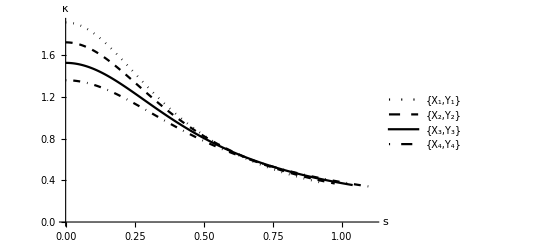

```mathematica
ListLinePlot[{HPCurvatureofLoC[180,923,1],HPCurvatureofLoC[360,975,1],HPCurvatureofLoC[540,1040,1],HPCurvatureofLoC[720,1112,1]},AxesLabel->{"s","κ"},PlotStyle->{{Dotted,Black},{Dashed,Black},{Black},{DotDashed,Black}},PlotLegends->LineLegend[{{{"X_1,Y_1"},{"X_2,Y_2"},{"X_3,Y_3"},{"X_4,Y_4"}}},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5]]
```

### Torsion

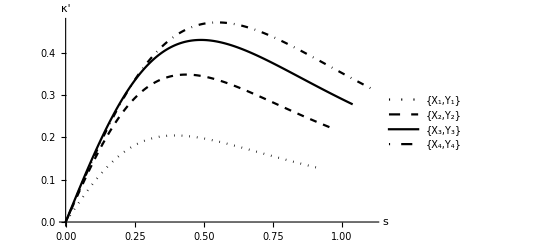

```mathematica
ListLinePlot[{HPTorsionofLoC[180,923,1],HPTorsionofLoC[360,975,1],HPTorsionofLoC[540,1040,1],HPTorsionofLoC[720,1112,1]},AxesLabel->{"s","κ'"},PlotStyle->{{Dotted,Black},{Dashed,Black},{Black},{DotDashed,Black}},PlotLegends->LineLegend[{{{"X_1,Y_1"},{"X_2,Y_2"},{"X_3,Y_3"},{"X_4,Y_4"}}},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5]]
```

### Derivative of Curvature

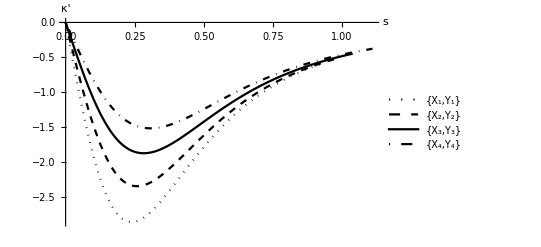

```mathematica
ListLinePlot[{HPDerivativeCurvatureofLoC[180,923,1],HPDerivativeCurvatureofLoC[360,975,1],HPDerivativeCurvatureofLoC[540,1040,1],HPDerivativeCurvatureofLoC[720,1112,1]},AxesLabel->{"s","κ'"},PlotStyle->{{Dotted,Black},{Dashed,Black},{Black},{DotDashed,Black}},PlotLegends->LineLegend[{{{"X_1,Y_1"},{"X_2,Y_2"},{"X_3,Y_3"},{"X_4,Y_4"}}},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5]]
```

### LCG

#### Set up

```mathematica
HPCurvatureofLoC2[v_,nn_,optimum_]:=Module[{opt1=optimum,xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2, d3tu1, d3tu2, xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2, d3tv1, d3tv2, D2uDs2, D2vDs2, GeoCur, Cur},
xu1=CUDAMemoryAllocate["Float",nn];
xu2=CUDAMemoryAllocate["Float",nn];
tu1=CUDAMemoryAllocate["Float",nn];
tu2=CUDAMemoryAllocate["Float",nn];
dtu1=CUDAMemoryAllocate["Float",nn];
dtu2=CUDAMemoryAllocate["Float",nn];
d2tu1=CUDAMemoryAllocate["Float",nn];
d2tu2=CUDAMemoryAllocate["Float",nn];
d3tu1=CUDAMemoryAllocate["Float",nn];
d3tu2=CUDAMemoryAllocate["Float",nn];
xv1=CUDAMemoryAllocate["Float",nn];
xv2=CUDAMemoryAllocate["Float",nn];
tv1=CUDAMemoryAllocate["Float",nn];
tv2=CUDAMemoryAllocate["Float",nn];
dtv1=CUDAMemoryAllocate["Float",nn];
dtv2=CUDAMemoryAllocate["Float",nn];
d2tv1=CUDAMemoryAllocate["Float",nn];
d2tv2=CUDAMemoryAllocate["Float",nn];
d3tv1=CUDAMemoryAllocate["Float",nn];
d3tv2=CUDAMemoryAllocate["Float",nn];
D2uDs2=CUDAMemoryAllocate["Float",nn];
D2vDs2=CUDAMemoryAllocate["Float",nn];
GeoCur=CUDAMemoryAllocate["Float",nn];
Cur=CUDAMemoryAllocate["Float",nn];

HPAllDetails[xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2, d3tu1, d3tu2, xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2, d3tv1, d3tv2, D2uDs2, D2vDs2, GeoCur,v,optimum,nn];
HPCurvature[Cur,xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2, d3tu1, d3tu2, xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2, d3tv1, d3tv2, D2uDs2, D2vDs2, GeoCur,optimum,nn];
CUDAMemoryGet[Cur]];
```

#### Four

```mathematica
1/HPCurvatureofLoC2[180,923,0]
```

{0.523043,0.523046,0.523055,0.523069,0.52309,0.523116,0.523148,0.523186,0.523229,0.523279,0.523334,0.523395,0.523462,0.523535,0.523614,0.523698,0.523789,0.523885,0.523987,0.524094,0.524208,0.524327,0.524452,0.524583,0.52472,0.524863,0.525011,0.525166,0.525326,0.525492,0.525663,0.525841,0.526024,0.526213,0.526408,0.526609,0.526816,0.527028,0.527247,0.52747,0.5277,0.527936,0.528177,0.528425,0.528678,0.528937,0.529201,0.529472,0.529748,0.53003,0.530318,0.530611,0.530911,0.531216,0.531527,0.531844,0.532167,0.532495,0.532829,0.533169,0.533515,0.533866,0.534224,0.534587,0.534956,0.53533,0.535711,0.536097,0.536489,0.536886,0.53729,0.537699,0.538114,0.538535,0.538961,0.539394,0.539832,0.540276,0.540725,0.541181,0.541642,0.542108,0.542581,0.543059,0.543543,0.544033,0.544529,0.54503,0.545537,0.54605,0.546568,0.547092,0.547622,0.548158,0.548699,0.549247,0.549799,0.550358,0.550922,0.551492,0.552068,0.552649,0.553236,0.553829,0.554428,0.555032,0.555642,0.556257,0.556879,0.557506,0.558138,0.558777,0.559421,0.56007,0.560726,0.561387,0.562054,0.562726,0.563404,0.564088,0.564777,0.565472,0.566173,0.566879,0.567591,0.568309,0.569032,0.569761,0.570496,0.571236,0.571982,0.572734,0.573491,0.574253,0.575022,0.575796,0.576576,0.577361,0.578152,0.578948,0.57975,0.580558,0.581371,0.58219,0.583015,0.583845,0.58468,0.585521,0.586368,0.587221,0.588079,0.588942,0.589811,0.590686,0.591566,0.592452,0.593344,0.59424,0.595143,0.596051,0.596965,0.597884,0.598808,0.599739,0.600674,0.601616,0.602562,0.603515,0.604473,0.605436,0.606405,0.607379,0.608359,0.609344,0.610335,0.611332,0.612334,0.613341,0.614354,0.615372,0.616396,0.617425,0.61846,0.6195,0.620546,0.621597,0.622654,0.623716,0.624783,0.625856,0.626935,0.628019,0.629108,0.630203,0.631303,0.632408,0.633519,0.634636,0.635758,0.636885,0.638018,0.639156,0.640299,0.641448,0.642602,0.643762,0.644927,0.646097,0.647273,0.648454,0.649641,0.650833,0.65203,0.653233,0.654441,0.655654,0.656873,0.658097,0.659326,0.660561,0.661801,0.663046,0.664297,0.665553,0.666815,0.668081,0.669353,0.670631,0.671913,0.673201,0.674494,0.675793,0.677096,0.678405,0.67972,0.681039,0.682364,0.683694,0.68503,0.68637,0.687716,0.689068,0.690424,0.691786,0.693153,0.694525,0.695902,0.697285,0.698673,0.700066,0.701464,0.702867,0.704276,0.70569,0.707109,0.708534,0.709963,0.711398,0.712837,0.714283,0.715733,0.717188,0.718649,0.720114,0.721585,0.723061,0.724543,0.726029,0.727521,0.729017,0.730519,0.732026,0.733538,0.735055,0.736577,0.738105,0.739637,0.741175,0.742718,0.744266,0.745819,0.747377,0.74894,0.750508,0.752081,0.75366,0.755243,0.756831,0.758425,0.760024,0.761627,0.763236,0.76485,0.766469,0.768093,0.769721,0.771355,0.772994,0.774638,0.776287,0.777941,0.7796,0.781264,0.782933,0.784608,0.786287,0.787971,0.78966,0.791353,0.793053,0.794756,0.796465,0.798179,0.799898,0.801622,0.803351,0.805084,0.806823,0.808566,0.810315,0.812069,0.813827,0.81559,0.817358,0.819132,0.82091,0.822693,0.82448,0.826273,0.828071,0.829874,0.831681,0.833493,0.835311,0.837133,0.83896,0.840791,0.842628,0.84447,0.846316,0.848168,0.850024,0.851885,0.85375,0.855621,0.857496,0.859377,0.861262,0.863152,0.865047,0.866946,0.868851,0.87076,0.872674,0.874592,0.876516,0.878444,0.880378,0.882315,0.884258,0.886206,0.888158,0.890115,0.892077,0.894043,0.896014,0.89799,0.899971,0.901957,0.903947,0.905942,0.907942,0.909946,0.911955,0.913969,0.915987,0.918011,0.920039,0.922071,0.924109,0.926151,0.928197,0.930249,0.932305,0.934366,0.936431,0.938502,0.940576,0.942656,0.94474,0.946828,0.948922,0.95102,0.953122,0.95523,0.957342,0.959458,0.961579,0.963705,0.965836,0.967971,0.97011,0.972255,0.974404,0.976557,0.978715,0.980878,0.983045,0.985217,0.987393,0.989574,0.99176,0.99395,0.996144,0.998343,1.00055,1.00276,1.00497,1.00719,1.00941,1.01163,1.01387,1.0161,1.01834,1.02059,1.02283,1.02509,1.02735,1.02961,1.03188,1.03415,1.03642,1.0387,1.04099,1.04328,1.04557,1.04787,1.05017,1.05248,1.05479,1.05711,1.05943,1.06176,1.06409,1.06642,1.06876,1.0711,1.07345,1.0758,1.07816,1.08052,1.08288,1.08525,1.08763,1.09001,1.09239,1.09478,1.09717,1.09956,1.10196,1.10437,1.10678,1.10919,1.11161,1.11403,1.11646,1.11889,1.12133,1.12377,1.12621,1.12866,1.13111,1.13357,1.13603,1.1385,1.14097,1.14344,1.14592,1.1484,1.15089,1.15338,1.15588,1.15838,1.16088,1.16339,1.16591,1.16842,1.17095,1.17347,1.176,1.17854,1.18108,1.18362,1.18617,1.18872,1.19127,1.19384,1.1964,1.19897,1.20154,1.20412,1.2067,1.20929,1.21188,1.21447,1.21707,1.21967,1.22228,1.22489,1.22751,1.23013,1.23275,1.23538,1.23801,1.24065,1.24329,1.24593,1.24858,1.25123,1.25389,1.25655,1.25922,1.26189,1.26456,1.26724,1.26992,1.27261,1.2753,1.27799,1.28069,1.2834,1.2861,1.28882,1.29153,1.29425,1.29697,1.2997,1.30243,1.30517,1.30791,1.31066,1.3134,1.31616,1.31891,1.32167,1.32444,1.32721,1.32998,1.33276,1.33554,1.33833,1.34111,1.34391,1.34671,1.34951,1.35231,1.35512,1.35794,1.36075,1.36358,1.3664,1.36923,1.37207,1.3749,1.37775,1.38059,1.38344,1.3863,1.38915,1.39202,1.39488,1.39775,1.40063,1.40351,1.40639,1.40927,1.41216,1.41506,1.41796,1.42086,1.42377,1.42668,1.42959,1.43251,1.43543,1.43836,1.44129,1.44422,1.44716,1.4501,1.45305,1.456,1.45895,1.46191,1.46487,1.46784,1.4708,1.47378,1.47676,1.47974,1.48272,1.48571,1.4887,1.4917,1.4947,1.49771,1.50072,1.50373,1.50675,1.50977,1.51279,1.51582,1.51885,1.52189,1.52493,1.52797,1.53102,1.53407,1.53713,1.54019,1.54325,1.54632,1.54939,1.55246,1.55554,1.55862,1.56171,1.5648,1.56789,1.57099,1.57409,1.5772,1.58031,1.58342,1.58654,1.58966,1.59278,1.59591,1.59904,1.60218,1.60532,1.60846,1.61161,1.61476,1.61792,1.62108,1.62424,1.62741,1.63058,1.63375,1.63693,1.64011,1.6433,1.64649,1.64968,1.65288,1.65608,1.65928,1.66249,1.6657,1.66892,1.67214,1.67536,1.67859,1.68182,1.68505,1.68829,1.69153,1.69478,1.69803,1.70128,1.70454,1.7078,1.71106,1.71433,1.7176,1.72087,1.72415,1.72744,1.73072,1.73401,1.73731,1.7406,1.74391,1.74721,1.75052,1.75383,1.75715,1.76047,1.76379,1.76712,1.77045,1.77378,1.77712,1.78046,1.78381,1.78716,1.79051,1.79387,1.79723,1.80059,1.80396,1.80733,1.8107,1.81408,1.81746,1.82085,1.82424,1.82763,1.83103,1.83443,1.83783,1.84124,1.84465,1.84807,1.85148,1.85491,1.85833,1.86176,1.86519,1.86863,1.87207,1.87551,1.87896,1.88241,1.88587,1.88932,1.89278,1.89625,1.89972,1.90319,1.90667,1.91015,1.91363,1.91712,1.92061,1.9241,1.9276,1.9311,1.9346,1.93811,1.94162,1.94514,1.94865,1.95218,1.9557,1.95923,1.96276,1.9663,1.96984,1.97338,1.97693,1.98048,1.98403,1.98759,1.99115,1.99472,1.99829,2.00186,2.00543,2.00901,2.01259,2.01618,2.01977,2.02336,2.02696,2.03056,2.03416,2.03777,2.04138,2.04499,2.04861,2.05223,2.05585,2.05948,2.06311,2.06674,2.07038,2.07402,2.07767,2.08132,2.08497,2.08862,2.09228,2.09594,2.09961,2.10328,2.10695,2.11063,2.11431,2.11799,2.12168,2.12537,2.12906,2.13276,2.13646,2.14016,2.14387,2.14758,2.15129,2.15501,2.15873,2.16245,2.16618,2.16991,2.17364,2.17738,2.18112,2.18487,2.18861,2.19237,2.19612,2.19988,2.20364,2.20741,2.21117,2.21495,2.21872,2.2225,2.22628,2.23007,2.23386,2.23765,2.24144,2.24524,2.24904,2.25285,2.25666,2.26047,2.26429,2.2681,2.27193,2.27575,2.27958,2.28341,2.28725,2.29109,2.29493,2.29878,2.30263,2.30648,2.31033,2.31419,2.31806,2.32192,2.32579,2.32966,2.33354,2.33742,2.3413,2.34519,2.34908,2.35297,2.35686,2.36076,2.36466,2.36857,2.37248,2.37639,2.38031,2.38423,2.38815,2.39207,2.396,2.39993,2.40387,2.40781,2.41175,2.4157,2.41964,2.4236,2.42755,2.43151,2.43547,2.43944,2.4434,2.44738,2.45135,2.45533,2.45931,2.46329,2.46728,2.47127,2.47527,2.47926,2.48327,2.48727,2.49128,2.49529,2.4993,2.50332,2.50734,2.51136,2.51539,2.51942,2.52345,2.52749,2.53153,2.53557,2.53962,2.54367,2.54772,2.55178,2.55583,2.5599,2.56396,2.56803,2.5721,2.57618,2.58026,2.58434,2.58842,2.59251,2.5966,2.6007,2.60479,2.60889,2.613,2.61711,2.62122,2.62533,2.62945,2.63357}

```mathematica
1/HPCurvatureofLoC2[360,975,0]
```

{0.581053,0.581056,0.581064,0.581078,0.581097,0.581121,0.581151,0.581187,0.581227,0.581274,0.581325,0.581383,0.581445,0.581514,0.581587,0.581666,0.581751,0.581841,0.581936,0.582037,0.582143,0.582255,0.582372,0.582495,0.582623,0.582756,0.582895,0.58304,0.583189,0.583345,0.583505,0.583672,0.583843,0.58402,0.584203,0.584391,0.584584,0.584783,0.584987,0.585197,0.585412,0.585632,0.585858,0.58609,0.586327,0.586569,0.586817,0.58707,0.587328,0.587592,0.587862,0.588136,0.588417,0.588702,0.588993,0.58929,0.589592,0.589899,0.590212,0.59053,0.590854,0.591182,0.591517,0.591857,0.592202,0.592552,0.592908,0.59327,0.593637,0.594009,0.594386,0.594769,0.595158,0.595551,0.595951,0.596355,0.596765,0.59718,0.597601,0.598027,0.598459,0.598896,0.599338,0.599785,0.600238,0.600697,0.60116,0.601629,0.602104,0.602584,0.603069,0.603559,0.604055,0.604556,0.605063,0.605575,0.606092,0.606615,0.607143,0.607676,0.608215,0.608759,0.609308,0.609863,0.610423,0.610988,0.611559,0.612135,0.612716,0.613302,0.613894,0.614492,0.615094,0.615702,0.616315,0.616933,0.617557,0.618186,0.618821,0.61946,0.620105,0.620755,0.621411,0.622072,0.622738,0.623409,0.624086,0.624768,0.625455,0.626147,0.626845,0.627548,0.628256,0.62897,0.629688,0.630412,0.631142,0.631876,0.632616,0.633361,0.634111,0.634866,0.635627,0.636393,0.637164,0.63794,0.638722,0.639509,0.640301,0.641098,0.6419,0.642708,0.64352,0.644338,0.645162,0.64599,0.646823,0.647662,0.648506,0.649355,0.650209,0.651069,0.651934,0.652803,0.653678,0.654558,0.655444,0.656334,0.657229,0.65813,0.659036,0.659947,0.660863,0.661784,0.66271,0.663642,0.664579,0.66552,0.666467,0.667419,0.668376,0.669338,0.670305,0.671278,0.672255,0.673238,0.674225,0.675218,0.676216,0.677218,0.678226,0.679239,0.680257,0.68128,0.682309,0.683342,0.68438,0.685423,0.686472,0.687525,0.688583,0.689647,0.690715,0.691789,0.692867,0.693951,0.695039,0.696133,0.697231,0.698335,0.699443,0.700557,0.701675,0.702798,0.703927,0.70506,0.706199,0.707342,0.70849,0.709644,0.710802,0.711965,0.713133,0.714306,0.715484,0.716667,0.717855,0.719048,0.720246,0.721448,0.722656,0.723868,0.725086,0.726308,0.727535,0.728767,0.730004,0.731246,0.732492,0.733744,0.735,0.736262,0.737528,0.738799,0.740075,0.741356,0.742641,0.743932,0.745227,0.746527,0.747832,0.749142,0.750457,0.751776,0.7531,0.754429,0.755763,0.757102,0.758445,0.759794,0.761147,0.762505,0.763867,0.765234,0.766607,0.767984,0.769365,0.770752,0.772143,0.773539,0.77494,0.776345,0.777755,0.77917,0.78059,0.782014,0.783443,0.784877,0.786316,0.787759,0.789207,0.790659,0.792117,0.793579,0.795045,0.796517,0.797993,0.799474,0.800959,0.802449,0.803944,0.805443,0.806947,0.808456,0.809969,0.811487,0.81301,0.814537,0.816068,0.817605,0.819146,0.820692,0.822242,0.823797,0.825356,0.82692,0.828489,0.830062,0.83164,0.833222,0.834809,0.836401,0.837997,0.839598,0.841203,0.842812,0.844427,0.846046,0.847669,0.849297,0.850929,0.852566,0.854208,0.855854,0.857504,0.859159,0.860819,0.862483,0.864151,0.865824,0.867502,0.869184,0.87087,0.872561,0.874256,0.875956,0.87766,0.879369,0.881082,0.882799,0.884521,0.886248,0.887979,0.889714,0.891454,0.893198,0.894946,0.896699,0.898457,0.900218,0.901985,0.903755,0.90553,0.907309,0.909093,0.910881,0.912673,0.91447,0.916271,0.918077,0.919886,0.921701,0.923519,0.925342,0.927169,0.929001,0.930836,0.932677,0.934521,0.93637,0.938223,0.94008,0.941942,0.943808,0.945678,0.947553,0.949431,0.951314,0.953202,0.955093,0.956989,0.95889,0.960794,0.962702,0.964615,0.966532,0.968454,0.970379,0.972309,0.974243,0.976181,0.978124,0.98007,0.982021,0.983976,0.985936,0.987899,0.989867,0.991838,0.993814,0.995795,0.997779,0.999767,1.00176,1.00376,1.00576,1.00776,1.00977,1.01179,1.0138,1.01582,1.01785,1.01988,1.02191,1.02395,1.026,1.02804,1.03009,1.03215,1.03421,1.03627,1.03833,1.04041,1.04248,1.04456,1.04664,1.04873,1.05082,1.05292,1.05502,1.05712,1.05923,1.06134,1.06345,1.06557,1.0677,1.06982,1.07196,1.07409,1.07623,1.07837,1.08052,1.08267,1.08483,1.08699,1.08915,1.09132,1.09349,1.09567,1.09785,1.10003,1.10222,1.10441,1.1066,1.1088,1.11101,1.11321,1.11543,1.11764,1.11986,1.12208,1.12431,1.12654,1.12877,1.13101,1.13326,1.1355,1.13775,1.14001,1.14226,1.14453,1.14679,1.14906,1.15133,1.15361,1.15589,1.15818,1.16047,1.16276,1.16506,1.16736,1.16966,1.17197,1.17428,1.1766,1.17892,1.18124,1.18357,1.1859,1.18823,1.19057,1.19292,1.19526,1.19761,1.19997,1.20232,1.20469,1.20705,1.20942,1.21179,1.21417,1.21655,1.21893,1.22132,1.22371,1.22611,1.22851,1.23091,1.23332,1.23573,1.23814,1.24056,1.24298,1.24541,1.24784,1.25027,1.2527,1.25514,1.25759,1.26004,1.26249,1.26494,1.2674,1.26986,1.27233,1.2748,1.27727,1.27975,1.28223,1.28471,1.2872,1.28969,1.29219,1.29469,1.29719,1.2997,1.30221,1.30472,1.30724,1.30976,1.31228,1.31481,1.31734,1.31988,1.32241,1.32496,1.3275,1.33005,1.3326,1.33516,1.33772,1.34029,1.34285,1.34542,1.348,1.35058,1.35316,1.35574,1.35833,1.36093,1.36352,1.36612,1.36872,1.37133,1.37394,1.37655,1.37917,1.38179,1.38442,1.38704,1.38968,1.39231,1.39495,1.39759,1.40024,1.40289,1.40554,1.40819,1.41085,1.41352,1.41618,1.41885,1.42153,1.4242,1.42688,1.42957,1.43225,1.43494,1.43764,1.44034,1.44304,1.44574,1.44845,1.45116,1.45388,1.45659,1.45932,1.46204,1.46477,1.4675,1.47024,1.47298,1.47572,1.47846,1.48121,1.48396,1.48672,1.48948,1.49224,1.49501,1.49778,1.50055,1.50333,1.50611,1.50889,1.51168,1.51447,1.51726,1.52006,1.52286,1.52566,1.52847,1.53127,1.53409,1.5369,1.53972,1.54255,1.54537,1.5482,1.55104,1.55387,1.55671,1.55956,1.5624,1.56525,1.56811,1.57096,1.57382,1.57669,1.57955,1.58242,1.5853,1.58817,1.59105,1.59394,1.59682,1.59971,1.6026,1.6055,1.6084,1.6113,1.61421,1.61712,1.62003,1.62295,1.62586,1.62879,1.63171,1.63464,1.63757,1.64051,1.64345,1.64639,1.64933,1.65228,1.65523,1.65819,1.66115,1.66411,1.66707,1.67004,1.67301,1.67598,1.67896,1.68194,1.68493,1.68791,1.6909,1.6939,1.69689,1.69989,1.70289,1.7059,1.70891,1.71192,1.71494,1.71796,1.72098,1.724,1.72703,1.73006,1.7331,1.73613,1.73917,1.74222,1.74527,1.74832,1.75137,1.75443,1.75749,1.76055,1.76361,1.76668,1.76976,1.77283,1.77591,1.77899,1.78208,1.78516,1.78826,1.79135,1.79445,1.79755,1.80065,1.80376,1.80687,1.80998,1.8131,1.81621,1.81934,1.82246,1.82559,1.82872,1.83186,1.83499,1.83813,1.84128,1.84442,1.84757,1.85073,1.85388,1.85704,1.8602,1.86337,1.86654,1.86971,1.87288,1.87606,1.87924,1.88242,1.88561,1.8888,1.89199,1.89519,1.89839,1.90159,1.90479,1.908,1.91121,1.91442,1.91764,1.92086,1.92408,1.92731,1.93054,1.93377,1.93701,1.94024,1.94348,1.94673,1.94997,1.95322,1.95648,1.95973,1.96299,1.96625,1.96952,1.97279,1.97606,1.97933,1.98261,1.98589,1.98917,1.99245,1.99574,1.99903,2.00233,2.00563,2.00893,2.01223,2.01554,2.01885,2.02216,2.02547,2.02879,2.03211,2.03544,2.03876,2.04209,2.04543,2.04876,2.0521,2.05544,2.05879,2.06213,2.06548,2.06884,2.07219,2.07555,2.07891,2.08228,2.08565,2.08902,2.09239,2.09577,2.09915,2.10253,2.10591,2.1093,2.11269,2.11609,2.11948,2.12288,2.12629,2.12969,2.1331,2.13651,2.13993,2.14334,2.14676,2.15019,2.15361,2.15704,2.16047,2.1639,2.16734,2.17078,2.17423,2.17767,2.18112,2.18457,2.18802,2.19148,2.19494,2.1984,2.20187,2.20534,2.20881,2.21228,2.21576,2.21924,2.22272,2.22621,2.2297,2.23319,2.23668,2.24018,2.24368,2.24718,2.25068,2.25419,2.2577,2.26122,2.26473,2.26825,2.27177,2.2753,2.27883,2.28236,2.28589,2.28943,2.29297,2.29651,2.30005,2.3036,2.30715,2.3107,2.31426,2.31781,2.32138,2.32494,2.32851,2.33208,2.33565,2.33922,2.3428,2.34638,2.34997,2.35355,2.35714,2.36073,2.36433,2.36792,2.37152,2.37513,2.37873,2.38234,2.38595,2.38956,2.39318,2.3968,2.40042,2.40405,2.40767,2.4113,2.41494,2.41857,2.42221,2.42585,2.42949,2.43314,2.43679,2.44044,2.4441,2.44775,2.45141,2.45508,2.45874,2.46241,2.46608,2.46975,2.47343,2.47711,2.48079,2.48448,2.48816,2.49185,2.49555,2.49924,2.50294,2.50664,2.51034,2.51405,2.51776,2.52147,2.52518,2.5289,2.53262,2.53634,2.54007,2.54379,2.54752,2.55126,2.55499,2.55873,2.56247,2.56621,2.56996,2.57371,2.57746,2.58121,2.58497,2.58873,2.59249,2.59626,2.60003,2.6038,2.60757,2.61134,2.61512,2.6189,2.62269,2.62647,2.63026,2.63405,2.63784,2.64164,2.64544,2.64924,2.65305,2.65685,2.66066,2.66448,2.66829,2.67211,2.67593,2.67975,2.68358,2.68741,2.69124,2.69507,2.69891,2.70274,2.70659,2.71043}

```mathematica
1/HPCurvatureofLoC2[540,1040,0]
```

{0.655888,0.65589,0.655898,0.655911,0.655928,0.655951,0.655979,0.656012,0.65605,0.656093,0.656141,0.656195,0.656253,0.656317,0.656385,0.656458,0.656537,0.656621,0.65671,0.656803,0.656902,0.657006,0.657115,0.65723,0.657349,0.657473,0.657602,0.657737,0.657876,0.658021,0.65817,0.658325,0.658485,0.658649,0.658819,0.658994,0.659174,0.659359,0.659549,0.659744,0.659945,0.66015,0.66036,0.660576,0.660796,0.661022,0.661252,0.661488,0.661728,0.661974,0.662225,0.66248,0.662741,0.663007,0.663278,0.663554,0.663835,0.664121,0.664412,0.664708,0.665009,0.665316,0.665627,0.665943,0.666264,0.666591,0.666922,0.667258,0.6676,0.667946,0.668298,0.668654,0.669015,0.669382,0.669754,0.67013,0.670512,0.670898,0.67129,0.671686,0.672088,0.672495,0.672906,0.673323,0.673744,0.674171,0.674603,0.675039,0.675481,0.675928,0.676379,0.676836,0.677297,0.677764,0.678235,0.678712,0.679193,0.67968,0.680171,0.680668,0.681169,0.681675,0.682187,0.682703,0.683224,0.68375,0.684281,0.684818,0.685359,0.685905,0.686456,0.687012,0.687572,0.688138,0.688709,0.689285,0.689865,0.690451,0.691041,0.691637,0.692237,0.692842,0.693453,0.694068,0.694688,0.695313,0.695942,0.696577,0.697217,0.697861,0.698511,0.699165,0.699825,0.700489,0.701158,0.701832,0.702511,0.703194,0.703883,0.704576,0.705275,0.705978,0.706686,0.707399,0.708117,0.708839,0.709567,0.710299,0.711036,0.711778,0.712525,0.713277,0.714034,0.714795,0.715561,0.716333,0.717108,0.717889,0.718675,0.719465,0.72026,0.72106,0.721865,0.722675,0.723489,0.724309,0.725133,0.725962,0.726795,0.727634,0.728477,0.729325,0.730177,0.731035,0.731897,0.732764,0.733636,0.734513,0.735394,0.73628,0.737171,0.738067,0.738967,0.739872,0.740782,0.741697,0.742616,0.74354,0.744469,0.745402,0.74634,0.747283,0.748231,0.749183,0.75014,0.751102,0.752068,0.753039,0.754015,0.754995,0.75598,0.75697,0.757965,0.758964,0.759968,0.760976,0.761989,0.763007,0.764029,0.765057,0.766088,0.767125,0.768166,0.769211,0.770261,0.771316,0.772376,0.77344,0.774509,0.775582,0.77666,0.777742,0.77883,0.779921,0.781018,0.782118,0.783224,0.784334,0.785449,0.786568,0.787692,0.78882,0.789953,0.79109,0.792232,0.793379,0.79453,0.795685,0.796845,0.79801,0.799179,0.800353,0.801531,0.802714,0.803901,0.805093,0.806289,0.80749,0.808695,0.809904,0.811119,0.812337,0.81356,0.814788,0.81602,0.817256,0.818498,0.819743,0.820993,0.822247,0.823506,0.824769,0.826037,0.827309,0.828585,0.829866,0.831151,0.832441,0.833735,0.835034,0.836336,0.837644,0.838955,0.840271,0.841592,0.842917,0.844246,0.845579,0.846917,0.848259,0.849606,0.850957,0.852312,0.853672,0.855036,0.856404,0.857777,0.859154,0.860535,0.861921,0.86331,0.864704,0.866103,0.867506,0.868913,0.870324,0.87174,0.87316,0.874584,0.876012,0.877445,0.878882,0.880323,0.881768,0.883218,0.884672,0.88613,0.887592,0.889059,0.89053,0.892005,0.893484,0.894968,0.896455,0.897947,0.899443,0.900943,0.902448,0.903956,0.905469,0.906986,0.908507,0.910032,0.911562,0.913095,0.914633,0.916175,0.917721,0.919271,0.920825,0.922383,0.923946,0.925512,0.927083,0.928658,0.930237,0.93182,0.933407,0.934998,0.936593,0.938192,0.939796,0.941403,0.943015,0.94463,0.94625,0.947873,0.949501,0.951133,0.952769,0.954408,0.956052,0.9577,0.959352,0.961008,0.962668,0.964332,0.965999,0.967671,0.969347,0.971027,0.97271,0.974398,0.97609,0.977786,0.979485,0.981189,0.982897,0.984608,0.986323,0.988043,0.989766,0.991493,0.993224,0.994959,0.996698,0.998441,1.00019,1.00194,1.00369,1.00545,1.00721,1.00898,1.01075,1.01252,1.0143,1.01608,1.01787,1.01966,1.02145,1.02325,1.02505,1.02685,1.02866,1.03047,1.03229,1.03411,1.03593,1.03776,1.03959,1.04143,1.04327,1.04511,1.04696,1.04881,1.05066,1.05252,1.05438,1.05625,1.05811,1.05999,1.06186,1.06374,1.06563,1.06752,1.06941,1.0713,1.0732,1.0751,1.07701,1.07892,1.08083,1.08275,1.08467,1.0866,1.08853,1.09046,1.09239,1.09433,1.09628,1.09822,1.10017,1.10213,1.10409,1.10605,1.10801,1.10998,1.11195,1.11393,1.11591,1.11789,1.11988,1.12187,1.12386,1.12586,1.12786,1.12986,1.13187,1.13388,1.1359,1.13792,1.13994,1.14197,1.144,1.14603,1.14807,1.15011,1.15215,1.1542,1.15625,1.1583,1.16036,1.16242,1.16449,1.16655,1.16863,1.1707,1.17278,1.17486,1.17695,1.17904,1.18113,1.18322,1.18532,1.18743,1.18953,1.19164,1.19376,1.19587,1.19799,1.20012,1.20224,1.20438,1.20651,1.20865,1.21079,1.21293,1.21508,1.21723,1.21938,1.22154,1.2237,1.22587,1.22803,1.23021,1.23238,1.23456,1.23674,1.23892,1.24111,1.2433,1.2455,1.2477,1.2499,1.2521,1.25431,1.25652,1.25874,1.26095,1.26317,1.2654,1.26763,1.26986,1.27209,1.27433,1.27657,1.27882,1.28106,1.28331,1.28557,1.28783,1.29009,1.29235,1.29462,1.29689,1.29916,1.30144,1.30372,1.306,1.30829,1.31058,1.31287,1.31517,1.31747,1.31977,1.32207,1.32438,1.32669,1.32901,1.33133,1.33365,1.33597,1.3383,1.34063,1.34297,1.34531,1.34765,1.34999,1.35234,1.35469,1.35704,1.3594,1.36176,1.36412,1.36648,1.36885,1.37123,1.3736,1.37598,1.37836,1.38074,1.38313,1.38552,1.38792,1.39031,1.39271,1.39512,1.39752,1.39993,1.40234,1.40476,1.40718,1.4096,1.41202,1.41445,1.41688,1.41931,1.42175,1.42419,1.42663,1.42908,1.43153,1.43398,1.43643,1.43889,1.44135,1.44382,1.44628,1.44875,1.45123,1.4537,1.45618,1.45866,1.46115,1.46364,1.46613,1.46862,1.47112,1.47362,1.47612,1.47862,1.48113,1.48364,1.48616,1.48868,1.4912,1.49372,1.49624,1.49877,1.50131,1.50384,1.50638,1.50892,1.51146,1.51401,1.51656,1.51911,1.52167,1.52422,1.52679,1.52935,1.53192,1.53449,1.53706,1.53963,1.54221,1.54479,1.54738,1.54997,1.55255,1.55515,1.55774,1.56034,1.56294,1.56555,1.56815,1.57076,1.57338,1.57599,1.57861,1.58123,1.58385,1.58648,1.58911,1.59174,1.59438,1.59702,1.59966,1.6023,1.60495,1.60759,1.61025,1.6129,1.61556,1.61822,1.62088,1.62355,1.62622,1.62889,1.63156,1.63424,1.63692,1.6396,1.64229,1.64497,1.64766,1.65036,1.65305,1.65575,1.65845,1.66116,1.66386,1.66657,1.66929,1.672,1.67472,1.67744,1.68016,1.68289,1.68562,1.68835,1.69108,1.69382,1.69656,1.6993,1.70205,1.7048,1.70755,1.7103,1.71305,1.71581,1.71857,1.72134,1.7241,1.72687,1.72964,1.73242,1.73519,1.73797,1.74076,1.74354,1.74633,1.74912,1.75191,1.75471,1.75751,1.76031,1.76311,1.76592,1.76872,1.77154,1.77435,1.77717,1.77998,1.78281,1.78563,1.78846,1.79129,1.79412,1.79695,1.79979,1.80263,1.80547,1.80832,1.81116,1.81402,1.81687,1.81972,1.82258,1.82544,1.8283,1.83117,1.83404,1.83691,1.83978,1.84266,1.84554,1.84842,1.8513,1.85419,1.85708,1.85997,1.86286,1.86576,1.86865,1.87156,1.87446,1.87737,1.88027,1.88319,1.8861,1.88902,1.89194,1.89486,1.89778,1.90071,1.90364,1.90657,1.9095,1.91244,1.91538,1.91832,1.92126,1.92421,1.92716,1.93011,1.93306,1.93602,1.93898,1.94194,1.9449,1.94787,1.95084,1.95381,1.95678,1.95976,1.96274,1.96572,1.9687,1.97169,1.97467,1.97767,1.98066,1.98365,1.98665,1.98965,1.99266,1.99566,1.99867,2.00168,2.00469,2.00771,2.01072,2.01374,2.01677,2.01979,2.02282,2.02585,2.02888,2.03191,2.03495,2.03799,2.04103,2.04408,2.04712,2.05017,2.05322,2.05628,2.05933,2.06239,2.06545,2.06851,2.07158,2.07465,2.07772,2.08079,2.08387,2.08694,2.09002,2.09311,2.09619,2.09928,2.10237,2.10546,2.10855,2.11165,2.11475,2.11785,2.12095,2.12406,2.12716,2.13028,2.13339,2.1365,2.13962,2.14274,2.14586,2.14899,2.15211,2.15524,2.15837,2.16151,2.16464,2.16778,2.17092,2.17407,2.17721,2.18036,2.18351,2.18666,2.18982,2.19297,2.19613,2.19929,2.20246,2.20562,2.20879,2.21196,2.21514,2.21831,2.22149,2.22467,2.22785,2.23103,2.23422,2.23741,2.2406,2.24379,2.24699,2.25019,2.25339,2.25659,2.2598,2.263,2.26621,2.26943,2.27264,2.27586,2.27907,2.28229,2.28552,2.28874,2.29197,2.2952,2.29843,2.30167,2.3049,2.30814,2.31138,2.31463,2.31787,2.32112,2.32437,2.32762,2.33088,2.33413,2.33739,2.34065,2.34392,2.34718,2.35045,2.35372,2.35699,2.36027,2.36354,2.36682,2.3701,2.37339,2.37667,2.37996,2.38325,2.38654,2.38984,2.39313,2.39643,2.39973,2.40304,2.40634,2.40965,2.41296,2.41627,2.41958,2.4229,2.42622,2.42954,2.43286,2.43619,2.43952,2.44285,2.44618,2.44951,2.45285,2.45619,2.45953,2.46287,2.46621,2.46956,2.47291,2.47626,2.47961,2.48297,2.48633,2.48969,2.49305,2.49641,2.49978,2.50315,2.50652,2.50989,2.51327,2.51664,2.52002,2.5234,2.52679,2.53017,2.53356,2.53695,2.54034,2.54374,2.54713,2.55053,2.55393,2.55734,2.56074,2.56415,2.56756,2.57097,2.57438,2.5778,2.58121,2.58463,2.58806,2.59148,2.59491,2.59833,2.60176,2.6052,2.60863,2.61207,2.61551,2.61895,2.62239,2.62584,2.62928,2.63273,2.63618,2.63964,2.64309,2.64655,2.65001,2.65347,2.65694,2.6604,2.66387,2.66734,2.67081,2.67429,2.67777,2.68124,2.68473,2.68821,2.69169,2.69518,2.69867,2.70216,2.70566,2.70915,2.71265,2.71615,2.71965,2.72315,2.72666,2.73017,2.73368,2.73719,2.7407,2.74422,2.74774,2.75126,2.75478,2.7583,2.76183,2.76536,2.76889,2.77242,2.77596,2.77949,2.78303,2.78657,2.79011,2.79366,2.79721,2.80076,2.80431,2.80786,2.81141,2.81497,2.81853,2.82209,2.82566}

```mathematica
1/HPCurvatureofLoC2[720,1112,0]
```

{0.736269,0.736271,0.736279,0.73629,0.736307,0.736328,0.736355,0.736386,0.736421,0.736462,0.736507,0.736557,0.736611,0.736671,0.736735,0.736804,0.736877,0.736956,0.737039,0.737127,0.73722,0.737317,0.737419,0.737526,0.737638,0.737754,0.737875,0.738001,0.738132,0.738267,0.738407,0.738552,0.738702,0.738856,0.739015,0.739179,0.739348,0.739521,0.739699,0.739882,0.74007,0.740262,0.740459,0.740661,0.740867,0.741079,0.741295,0.741515,0.741741,0.741971,0.742206,0.742445,0.74269,0.742939,0.743193,0.743451,0.743715,0.743983,0.744255,0.744533,0.744815,0.745102,0.745394,0.74569,0.745991,0.746297,0.746607,0.746922,0.747242,0.747567,0.747896,0.74823,0.748569,0.748912,0.749261,0.749613,0.749971,0.750333,0.7507,0.751072,0.751448,0.751829,0.752215,0.752606,0.753001,0.753401,0.753805,0.754214,0.754628,0.755047,0.75547,0.755898,0.75633,0.756767,0.75721,0.757656,0.758107,0.758563,0.759024,0.759489,0.759959,0.760434,0.760913,0.761397,0.761886,0.762379,0.762877,0.763379,0.763886,0.764398,0.764915,0.765436,0.765962,0.766492,0.767027,0.767567,0.768111,0.76866,0.769214,0.769772,0.770335,0.770902,0.771474,0.772051,0.772632,0.773218,0.773809,0.774404,0.775004,0.775608,0.776217,0.776831,0.777449,0.778072,0.778699,0.779331,0.779967,0.780609,0.781254,0.781905,0.782559,0.783219,0.783883,0.784551,0.785225,0.785902,0.786585,0.787272,0.787963,0.788659,0.789359,0.790065,0.790774,0.791488,0.792207,0.79293,0.793658,0.79439,0.795127,0.795869,0.796615,0.797365,0.79812,0.798879,0.799644,0.800412,0.801185,0.801963,0.802744,0.803531,0.804322,0.805118,0.805918,0.806722,0.807531,0.808345,0.809163,0.809985,0.810812,0.811643,0.812479,0.81332,0.814164,0.815014,0.815867,0.816725,0.817588,0.818455,0.819327,0.820203,0.821083,0.821968,0.822857,0.823751,0.824649,0.825551,0.826458,0.82737,0.828285,0.829205,0.83013,0.831059,0.831992,0.83293,0.833872,0.834819,0.83577,0.836725,0.837685,0.838649,0.839617,0.84059,0.841567,0.842549,0.843534,0.844525,0.845519,0.846518,0.847521,0.848529,0.849541,0.850557,0.851578,0.852603,0.853632,0.854666,0.855703,0.856746,0.857792,0.858843,0.859898,0.860957,0.862021,0.863089,0.864161,0.865238,0.866318,0.867403,0.868493,0.869586,0.870684,0.871786,0.872893,0.874003,0.875118,0.876237,0.877361,0.878488,0.87962,0.880756,0.881896,0.883041,0.884189,0.885342,0.886499,0.887661,0.888826,0.889996,0.89117,0.892348,0.89353,0.894716,0.895907,0.897102,0.898301,0.899504,0.900711,0.901922,0.903138,0.904358,0.905581,0.906809,0.908041,0.909278,0.910518,0.911763,0.913011,0.914264,0.915521,0.916782,0.918047,0.919316,0.920589,0.921866,0.923147,0.924433,0.925722,0.927016,0.928313,0.929615,0.930921,0.932231,0.933544,0.934862,0.936184,0.93751,0.93884,0.940174,0.941512,0.942854,0.9442,0.94555,0.946904,0.948262,0.949624,0.95099,0.95236,0.953734,0.955112,0.956494,0.95788,0.95927,0.960664,0.962062,0.963463,0.964869,0.966278,0.967692,0.96911,0.970531,0.971956,0.973385,0.974819,0.976256,0.977697,0.979142,0.98059,0.982043,0.983499,0.98496,0.986424,0.987892,0.989364,0.99084,0.99232,0.993804,0.995291,0.996782,0.998277,0.999776,1.00128,1.00279,1.0043,1.00581,1.00733,1.00885,1.01038,1.01191,1.01344,1.01498,1.01652,1.01806,1.01961,1.02116,1.02272,1.02428,1.02584,1.02741,1.02898,1.03055,1.03213,1.03371,1.0353,1.03689,1.03848,1.04008,1.04168,1.04328,1.04489,1.0465,1.04812,1.04974,1.05136,1.05299,1.05462,1.05625,1.05789,1.05953,1.06117,1.06282,1.06447,1.06613,1.06779,1.06945,1.07112,1.07279,1.07446,1.07614,1.07782,1.07951,1.08119,1.08289,1.08458,1.08628,1.08798,1.08969,1.0914,1.09311,1.09483,1.09655,1.09827,1.1,1.10173,1.10346,1.1052,1.10694,1.10869,1.11044,1.11219,1.11395,1.1157,1.11747,1.11923,1.121,1.12277,1.12455,1.12633,1.12811,1.1299,1.13169,1.13348,1.13528,1.13708,1.13889,1.14069,1.1425,1.14432,1.14614,1.14796,1.14978,1.15161,1.15344,1.15528,1.15711,1.15895,1.1608,1.16265,1.1645,1.16635,1.16821,1.17007,1.17194,1.17381,1.17568,1.17755,1.17943,1.18131,1.1832,1.18509,1.18698,1.18887,1.19077,1.19267,1.19458,1.19648,1.19839,1.20031,1.20223,1.20415,1.20607,1.208,1.20993,1.21186,1.2138,1.21574,1.21769,1.21963,1.22158,1.22354,1.22549,1.22745,1.22942,1.23138,1.23335,1.23532,1.2373,1.23928,1.24126,1.24325,1.24523,1.24723,1.24922,1.25122,1.25322,1.25522,1.25723,1.25924,1.26125,1.26327,1.26529,1.26731,1.26934,1.27137,1.2734,1.27544,1.27747,1.27952,1.28156,1.28361,1.28566,1.28771,1.28977,1.29183,1.29389,1.29596,1.29803,1.3001,1.30217,1.30425,1.30633,1.30842,1.31051,1.3126,1.31469,1.31678,1.31888,1.32099,1.32309,1.3252,1.32731,1.32942,1.33154,1.33366,1.33578,1.33791,1.34004,1.34217,1.34431,1.34644,1.34859,1.35073,1.35288,1.35502,1.35718,1.35933,1.36149,1.36365,1.36582,1.36798,1.37015,1.37233,1.3745,1.37668,1.37886,1.38104,1.38323,1.38542,1.38761,1.38981,1.39201,1.39421,1.39641,1.39862,1.40083,1.40304,1.40526,1.40748,1.4097,1.41192,1.41415,1.41638,1.41861,1.42085,1.42308,1.42532,1.42757,1.42981,1.43206,1.43431,1.43657,1.43883,1.44109,1.44335,1.44561,1.44788,1.45015,1.45243,1.4547,1.45698,1.45926,1.46155,1.46384,1.46613,1.46842,1.47071,1.47301,1.47531,1.47762,1.47992,1.48223,1.48454,1.48686,1.48917,1.49149,1.49382,1.49614,1.49847,1.5008,1.50313,1.50547,1.50781,1.51015,1.51249,1.51484,1.51718,1.51954,1.52189,1.52425,1.5266,1.52897,1.53133,1.5337,1.53607,1.53844,1.54081,1.54319,1.54557,1.54795,1.55034,1.55272,1.55511,1.55751,1.5599,1.5623,1.5647,1.5671,1.56951,1.57192,1.57433,1.57674,1.57915,1.58157,1.58399,1.58642,1.58884,1.59127,1.5937,1.59613,1.59857,1.60101,1.60345,1.60589,1.60833,1.61078,1.61323,1.61568,1.61814,1.6206,1.62306,1.62552,1.62798,1.63045,1.63292,1.63539,1.63787,1.64035,1.64283,1.64531,1.64779,1.65028,1.65277,1.65526,1.65775,1.66025,1.66275,1.66525,1.66776,1.67026,1.67277,1.67528,1.67779,1.68031,1.68283,1.68535,1.68787,1.6904,1.69292,1.69545,1.69798,1.70052,1.70306,1.7056,1.70814,1.71068,1.71323,1.71578,1.71833,1.72088,1.72344,1.72599,1.72855,1.73112,1.73368,1.73625,1.73882,1.74139,1.74396,1.74654,1.74912,1.7517,1.75428,1.75687,1.75945,1.76204,1.76464,1.76723,1.76983,1.77243,1.77503,1.77763,1.78024,1.78285,1.78546,1.78807,1.79068,1.7933,1.79592,1.79854,1.80116,1.80379,1.80642,1.80905,1.81168,1.81432,1.81695,1.81959,1.82223,1.82488,1.82752,1.83017,1.83282,1.83547,1.83813,1.84078,1.84344,1.8461,1.84877,1.85143,1.8541,1.85677,1.85944,1.86212,1.86479,1.86747,1.87015,1.87283,1.87552,1.87821,1.88089,1.88359,1.88628,1.88898,1.89167,1.89437,1.89707,1.89978,1.90249,1.90519,1.9079,1.91062,1.91333,1.91605,1.91877,1.92149,1.92421,1.92694,1.92966,1.93239,1.93512,1.93786,1.94059,1.94333,1.94607,1.94881,1.95156,1.9543,1.95705,1.9598,1.96255,1.96531,1.96806,1.97082,1.97358,1.97634,1.97911,1.98187,1.98464,1.98741,1.99019,1.99296,1.99574,1.99852,2.0013,2.00408,2.00687,2.00965,2.01244,2.01523,2.01803,2.02082,2.02362,2.02642,2.02922,2.03202,2.03483,2.03763,2.04044,2.04325,2.04607,2.04888,2.0517,2.05452,2.05734,2.06016,2.06298,2.06581,2.06864,2.07147,2.0743,2.07714,2.07997,2.08281,2.08565,2.0885,2.09134,2.09419,2.09704,2.09989,2.10274,2.10559,2.10845,2.11131,2.11417,2.11703,2.11989,2.12276,2.12563,2.1285,2.13137,2.13424,2.13712,2.14,2.14287,2.14576,2.14864,2.15152,2.15441,2.1573,2.16019,2.16308,2.16598,2.16888,2.17177,2.17467,2.17758,2.18048,2.18339,2.18629,2.1892,2.19212,2.19503,2.19794,2.20086,2.20378,2.2067,2.20963,2.21255,2.21548,2.21841,2.22134,2.22427,2.2272,2.23014,2.23308,2.23602,2.23896,2.2419,2.24485,2.24779,2.25074,2.25369,2.25665,2.2596,2.26256,2.26552,2.26848,2.27144,2.2744,2.27737,2.28033,2.2833,2.28627,2.28925,2.29222,2.2952,2.29818,2.30116,2.30414,2.30712,2.31011,2.31309,2.31608,2.31908,2.32207,2.32506,2.32806,2.33106,2.33406,2.33706,2.34006,2.34307,2.34608,2.34908,2.3521,2.35511,2.35812,2.36114,2.36416,2.36718,2.3702,2.37322,2.37625,2.37927,2.3823,2.38533,2.38836,2.3914,2.39443,2.39747,2.40051,2.40355,2.40659,2.40964,2.41269,2.41573,2.41878,2.42183,2.42489,2.42794,2.431,2.43406,2.43712,2.44018,2.44324,2.44631,2.44938,2.45245,2.45552,2.45859,2.46166,2.46474,2.46782,2.4709,2.47398,2.47706,2.48015,2.48323,2.48632,2.48941,2.4925,2.4956,2.49869,2.50179,2.50489,2.50799,2.51109,2.51419,2.5173,2.5204,2.52351,2.52662,2.52973,2.53285,2.53596,2.53908,2.5422,2.54532,2.54844,2.55157,2.55469,2.55782,2.56095,2.56408,2.56721,2.57035,2.57348,2.57662,2.57976,2.5829,2.58604,2.58919,2.59233,2.59548,2.59863,2.60178,2.60493,2.60809,2.61125,2.6144,2.61756,2.62072,2.62389,2.62705,2.63022,2.63338,2.63655,2.63972,2.6429,2.64607,2.64925,2.65243,2.6556,2.65879,2.66197,2.66515,2.66834,2.67153,2.67471,2.6779,2.6811,2.68429,2.68749,2.69069,2.69389,2.69709,2.70029,2.70349,2.7067,2.70991,2.71311,2.71633,2.71954,2.72275,2.72597,2.72919,2.7324,2.73562,2.73885,2.74207,2.7453,2.74852,2.75175,2.75498,2.75821,2.76145,2.76468,2.76792,2.77116,2.7744,2.77764,2.78088,2.78413,2.78737,2.79062,2.79387,2.79712,2.80037,2.80363,2.80688,2.81014,2.8134,2.81666,2.81992,2.82319,2.82645,2.82972,2.83299,2.83626,2.83953,2.84281,2.84608,2.84936,2.85264,2.85592,2.8592,2.86248,2.86577,2.86905,2.87234,2.87563,2.87892,2.88222,2.88551,2.88881,2.8921,2.8954,2.8987,2.90201,2.90531,2.90862,2.91192,2.91523,2.91854,2.92185,2.92517,2.92848,2.9318,2.93512,2.93844,2.94176,2.94508,2.9484,2.95173,2.95506,2.95839,2.96172,2.96505,2.96838,2.97172,2.97506,2.97839,2.98173}

```mathematica
HP2rho180[s_]:={0.5230430594479403,0.5230459945954584,0.5230546697795766,0.523069248650644,0.5230896669592048,0.5231158934512358,0.5231478646225383,0.5231857783614371,0.5232294088004825,0.52327895465076,0.5233343539734718,0.5233954145449204,0.5234624016434081,0.5235352544669367,0.5236138144879833,0.5236982830021968,0.5237885676007926,0.5238846742863837,0.5239865767217409,0.5240943143949364,0.524207763449207,0.5243272917764275,0.5244524486209207,0.5245834716404014,0.5247202711183507,0.5248629874026997,0.5250113672244039,0.5251655845145728,0.5253258139783776,0.5254916715168388,0.5256634312217562,0.5258409397553324,0.5260243735806664,0.5262134478941853,0.5264084059597312,0.5266092937669246,0.5268157938829992,0.5270282504489436,0.5272465119904062,0.5274704932208479,0.5277003412755873,0.5279359383459823,0.5281773660794676,0.528424673476686,0.5286777101544833,0.5289365589483173,0.529201269965759,0.5294716599185173,0.5297479465387415,0.5300299469224982,0.5303178129680365,0.5306114290528804,0.5309108809665473,0.5312160197262663,0.5315271337987724,0.531843906377911,0.532166559613021,0.5324949114175633,0.532829083702665,0.5331689959658024,0.5335147372445923,0.5338662614295137,0.5342235564813854,0.5345865765149329,0.5349555144795164,0.5353301205643507,0.5357105201564994,0.5360967025859934,0.5364886230829181,0.5368863743275807,0.5372898777517138,0.5376990890417201,0.5381141709806336,0.5385349073145754,0.5389614615873551,0.5393937211611171,0.5398317813543725,0.5402757035505418,0.5407252012343988,0.5411805099076015,0.5416415171578408,0.542108390296472,0.5425810172630842,0.5430593205932098,0.5435433985808118,0.5440331387373327,0.5445287107399595,0.5450299670036473,0.5455370073988134,0.5460497905593871,0.5465682393894412,0.5470924904736957,0.5476223956364683,0.5481581281064045,0.548699467856345,0.5492465888680473,0.5497994144418324,0.5503579757479516,0.5509222681903804,0.5514922147802612,0.5520678470374836,0.5526492333008826,0.5532362966878004,0.5538291791893104,0.5544276943659279,0.5550318379128081,0.5556417896330241,0.556257362183766,0.5568786624250122,0.5575056500843575,0.558138284639608,0.5587767114110814,0.559420666788039,0.5600704457198009,0.5607257463084387,0.561386827452048,0.5620535740009699,0.5627259830421655,0.5634040138753369,0.5640878530723547,0.5647771567564481,0.5654722638700872,0.5661730200043426,0.5668793458951396,0.5675913919650365,0.5683090406957149,0.5690323664237714,0.5697612894961374,0.5704959234736685,0.5712361886353756,0.5719820824666378,0.5727335242488777,0.5734905892626251,0.5742534322299312,0.5750218942157045,0.5757958936400581,0.5765755065685184,0.577360770160513,0.5781516024452359,0.5789480404187973,0.5797502016158432,0.5805577629023901,0.5813710824749698,0.5821899972738716,0.5830145044579516,0.5838446011303826,0.5846802435823831,0.5855214693094656,0.5863682752180198,0.5872207403541214,0.5880787385125098,0.5889422660066704,0.5898114019970855,0.5906860601574514,0.5915663199470478,0.5924521361902693,0.5933436309800254,0.5942404226763505,0.5951429694006022,0.5960510571536575,0.5969646391692859,0.5978837958649938,0.5988084803352285,0.5997385592504183,0.6006743276450991,0.6016156526924042,0.6025623998001948,0.6035146930931498,0.6044725710546072,0.6054359414654876,0.6064047984916449,0.6073791361128641,0.6083591687143876,0.6093444494073378,0.610335369092261,0.6113316999298929,0.6123336132481053,0.6133409685873444,0.6143538034737622,0.6153722009398197,0.6163959279374578,0.6174253389392197,0.6184600178874456,0.6195002749811738,0.6205459654157249,0.6215971725751168,0.6226537959570073,0.6237158726563835,0.6247833470513041,0.625856302676431,0.6269347303468003,0.6280186676023876,0.6291079164358055,0.6302027020123555,0.6313028248829073,0.6324084163629623,0.6335193702180325,0.63463586661387,0.6357577026224696,0.6368849623742759,0.6380175854351477,0.639155656418542,0.6402991632137696,0.6414480442949404,0.6426022370558511,0.6437619742137837,0.6449269462516031,0.6460974361079594,0.6472732312040863,0.6484543161563886,0.6496409770146142,0.6508328473906039,0.6520301634589853,0.6532327577312101,0.6544407153077162,0.6556541735874151,0.6568728603063931,0.6580967570608084,0.6593262077083858,0.6605609368576131,0.6618009780185657,0.6630464173941429,0.6642970792369468,0.6655531017421898,0.6668146249797299,0.6680811524376943,0.66935314117556,0.6706305188799427,0.6719131042554456,0.6732009290911909,0.674494079668959,0.6757925344838267,0.6770963807672719,0.6784053776793473,0.6797197210174799,0.6810393329350879,0.6823642451433064,0.6836943224394089,0.6850298188493672,0.6863703743826653,0.687716412472704,0.6890675705491457,0.6904240483242051,0.6917857631770359,0.6931526882054505,0.6945247383322629,0.6959021155367635,0.6972847349682982,0.6986726265529827,0.7000656451745623,0.7014638777721723,0.7028674124330311,0.704276101894347,0.7056899150019912,0.7071091774820764,0.708533501923029,0.7099629149973281,0.7113976245553133,0.7128374781216479,0.7142825029478622,0.7157327264778366,0.7171882376658634,0.718648695697467,0.7201144957434944,0.7215854805640656,0.7230614277531857,0.7245427368041378,0.7260291223205491,0.7275206725175742,0.7290172233913443,0.7305190532957232,0.7320259977799962,0.733537953552959,0.7350551374071433,0.7365774461019455,0.7381048393660467,0.7396374064344495,0.7411751068034731,0.7427178332768898,0.7442656747155928,0.7458185885988358,0.7473765980275784,0.74893972623898,0.7505078623152295,0.7520811629337287,0.7536595840258749,0.7552430805238025,0.7568314697814442,0.7584251829541016,0.7600236942048679,0.7616274366475496,0.7632361560652041,0.7648499423577626,0.7664687466421454,0.768092589286123,0.7697214907584143,0.7713554716292701,0.7729944101110808,0.7746383966923085,0.7762873794889164,0.7779413776298713,0.7796004103293099,0.7812644241246803,0.7829334374680043,0.7846075422743551,0.7862865369906568,0.7879705124255109,0.7896595607163994,0.7913534767313848,0.7930525014133614,0.7947562772478944,0.7964653477708324,0.7981792024114911,0.7998980079997353,0.8016219340278946,0.8033505372089155,0.8050842935484676,0.8068229886720183,0.8085664821820305,0.8103150223912027,0.8120685472480635,0.8138269144331948,0.8155901375192592,0.817358469019653,0.8191315257240215,0.8209097208610159,0.8226925871237739,0.8244804591752039,0.8262733517592988,0.8280708709375101,0.8298736008522108,0.8316810637131768,0.8334934356716488,0.8353105630449463,0.8371327904938626,0.8389597972560762,0.8407914252707066,0.8426281059991114,0.844469768200387,0.8463162537743746,0.8481675731466233,0.8500236505889949,0.8518845818644603,0.8537503773307232,0.8556210473233895,0.857496426846075,0.8593766999580997,0.8612618769137765,0.8631518791279834,0.8650466264286207,0.866946126634617,0.8688506574893631,0.8707596879526444,0.8726738576244456,0.8745924494403765,0.8765161072716098,0.8784444743009212,0.8803775567851169,0.8823154537163477,0.8842583588667092,0.8862057202609364,0.8881578222949148,0.8901149542374222,0.8920766513520926,0.8940430122035273,0.8960144240603238,0.897990415706885,0.8999711832690447,0.9019565382647325,0.9039468731556397,0.9059418044776287,0.9079416296890547,0.9099458617114876,0.9119549960868573,0.9139688399309627,0.9159874968251781,0.9180106701703504,0.9200386633908294,0.9220714810815374,0.9241087205392843,0.9261506875298233,0.9281973849923087,0.9302488157597657,0.9323049825577803,0.934365783928759,0.9364312209974904,0.938501504760413,0.940576111569268,0.942655567630691,0.9447397699745667,0.9468283999037438,0.94892188432182,0.9510199028551657,0.9531223458835723,0.9552297543661471,0.9573416954287737,0.9594582770554085,0.9615794987952471,0.9637052493429575,0.9658356376960388,0.9679707746632051,0.9701104363156747,0.9722547326759847,0.9744035492295418,0.9765569966785732,0.9787150733831429,0.9808776628553422,0.9830449920253501,0.9852165974649542,0.987393053414116,0.9895740103001195,0.991759581230667,0.9939496456674674,0.9961443174073815,0.9983434745285555,1.0005472315190087,1.00275558492466,1.0049684709203535,1.0071858849070963,1.0094077613715446,1.0116342775413087,1.0138652460690036,1.016100845423538,1.018340948081001,1.0205854241570682,1.0228347026026134,1.025088280367964,1.027346337401618,1.0296091831340441,1.0318760534585731,1.0341477005503836,1.0364239934532602,1.0387045415512994,1.040989786927764,1.0432793360160053,1.045573244338914,1.047871895578165,1.0501748912719615,1.0524825521128047,1.0547944085865208,1.0571107155004322,1.0594317990009,1.0617569829858435,1.0640866591876488,1.0664208872657561,1.068759727852952,1.0711027638909265,1.073450257734795,1.0758023383410902,1.078158582573565,1.0805194644603067,1.0828846275736816,1.0852542707605006,1.0876282437671736,1.090006606094343,1.0923896316193404,1.0947768131383533,1.0971685672478766,1.0995644530338595,1.1019648903543615,1.104369797517257,1.1067789453074055,1.1091926137727592,1.11161049860426,1.1140327339599645,1.1164597534982832,1.1188906552391946,1.121326170180727,1.123765913002334,1.1262102475959175,1.1286586330240982,1.1311114339755828,1.1335684853505203,1.1360302345235394,1.1384961322709588,1.1409662404969725,1.143440778034061,1.1459194196177622,1.1484026989888203,1.1508902117557218,1.1533821014891685,1.1558782753280796,1.1583785587904245,1.1608832563099942,1.1633923548971552,1.165905841302779,1.168423376523886,1.1709452694650482,1.173471341914385,1.1760019071495467,1.1785367043390342,1.1810758838349351,1.1836190140510707,1.1861665784317719,1.1887185634325912,1.1912747014839795,1.193835145137659,1.196399708309569,1.1989683730693887,1.201541637497471,1.2041189711930966,1.2067005289361292,1.209286381017252,1.2118765113950465,1.2144708158320017,1.217069364878893,1.2196722303030232,1.2222790398636183,1.2248903092251517,1.227505934234712,1.2301253579631903,1.2327491914894744,1.235377237688763,1.23800938740982,1.240645804878662,1.2432864728734792,1.2459312813544259,1.2485803042546444,1.251233430152212,1.2538909205923652,1.2565524769238685,1.2592182679693358,1.2618880857997636,1.264561909597311,1.267240483978871,1.2699229321043162,1.2726092310124284,1.275300035992537,1.2779947479258846,1.2806938329244688,1.2833969796306095,1.2861040686038037,1.288815572458895,1.2915311764468147,1.294250959875651,1.296974602368415,1.2997024829753716,1.3024346838618643,1.305170983988387,1.3079109546831877,1.3106552863952343,1.3134039615172974,1.316156652397046,1.318913233261153,1.3216740968683178,1.3244390152906518,1.327207966784234,1.329981034716204,1.3327584097664982,1.3355395416349112,1.3383250451899253,1.3411145808061693,1.3439078032000247,1.3467054423794567,1.3495071551030855,1.3523129194235965,1.355122603617647,1.3579364035504842,1.3607539665706707,1.363575931638236,1.3664019468350492,1.3692321013994029,1.3720659250501974,1.374904066498706,1.3777460538845583,1.3805924300368675,1.3834423778971352,1.3862966706089306,1.389154713924091,1.3920169432756873,1.394883105528362,1.3977535256643638,1.4006277155753022,1.4035058836146626,1.4063881237555318,1.4092744131997845,1.4121644910983102,1.4150586891345776,1.4179573445179543,1.4208597170410862,1.4237657793300929,1.4266758676168647,1.4295900801001526,1.4325080273891804,1.4354306647232375,1.4383564967446854,1.4412866038443206,1.4442204679999142,1.447158436578367,1.4501003613492596,1.4530462175685463,1.4559959801594138,1.4589501311925122,1.461907632014607,1.4648696014788731,1.467835378830424,1.4708049373243706,1.4737785087963953,1.4767559389655307,1.4797372016330965,1.482722663376444,1.4857119073711242,1.488704906407214,1.4917020308207616,1.4947031243499123,1.497708028270493,1.500716581376398,1.503729293850573,1.5067458722636866,1.5097662902513296,1.5127909303323526,1.5158189486584266,1.5188514129427433,1.5218873373383088,1.52492738350571,1.5279712497017321,1.5310190485628938,1.5340706140702192,1.5371256368036115,1.5401853578243245,1.5432484828950626,1.5463155499349712,1.5493863901221032,1.5524609756846859,1.5555398554090683,1.5586222837103818,1.561708520822202,1.564798977171689,1.5678930441003376,1.57099083889194,1.5740927761734003,1.5771980910668113,1.5803074952255585,1.5834205161354014,1.586537724113181,1.5896584936007523,1.5927837013910309,1.5959119610525254,1.5990444552844227,1.602180396486078,1.6053203671837204,1.6084643423472136,1.6116118321928024,1.6147632718415168,1.6179186352761512,1.6210775828833726,1.6242403988123457,1.6274068981880307,1.6305773687677652,1.6337514665303878,1.636929321312883,1.6401110650887054,1.6432965100698487,1.6464857888034519,1.6496788737922923,1.6528757372058946,1.6560760239367374,1.6592806863085046,1.6624888793936676,1.665700572111188,1.6689163970889587,1.672135330288572,1.6753586741260127,1.678585400046864,1.6818163181898969,1.685050728142054,1.6882884284447932,1.6915305790350101,1.6947759610181294,1.6980252272472407,1.70127817816616,1.704535130781789,1.7077958855444375,1.7110597164085322,1.7143279884019444,1.7175996257918982,1.7208747720462638,1.7241541045273852,1.7274365324286847,1.730722912322378,1.7340132178951746,1.7373070627141447,1.740604957480381,1.7439059706156095,1.7472113399710612,1.7505201305658145,1.753832126650619,1.7571480295153499,1.7604679970304224,1.7637912624018097,1.7671183502192411,1.7704492326498842,1.7737836940026224,1.7771218919171707,1.7804634196789138,1.7838091921820467,1.7871584248622845,1.7905108946868284,1.7938675262407353,1.79722733288663,1.8005910524752253,1.8039584642217719,1.8073293441246716,1.8107040512106316,1.8140819692391799,1.8174644417123789,1.8208502632856758,1.8242394008021026,1.8276320198488936,1.8310286882933433,1.8344287791129952,1.8378326626540933,1.8412403107581177,1.8446512893096594,1.8480661757132841,1.8514845344487343,1.854906128718015,1.8583311300295555,1.8617607455735896,1.8651932974418597,1.868629372377164,1.8720693570617515,1.8755132246741342,1.8789603167839046,1.882410810197044,1.8858650964553005,1.8893233602248105,1.8927845077294945,1.8962495724818702,1.8997185277750288,1.903190698909057,1.90666605146216,1.9101458555252908,1.913628562372116,1.9171154485840416,1.9206056108848408,1.9240987948991224,1.9275965144466771,1.931096971426993,1.9346014647755316,1.9381092974678178,1.9416206612535298,1.9451357508032263,1.9486540847280196,1.952176310540162,1.9557019453953879,1.9592311859531344,1.9627640022228072,1.9663003638962506,1.9698400090641766,1.9733838327403181,1.976930413463834,1.980481114844115,1.984034739377799,1.9875921916603236,1.9911529715590537,1.9947177576698212,1.9982858103881416,2.001857454478375,2.0054326599216927,2.009010915241954,2.012593150361697,2.016178854885962,2.0197679975330183,2.023360546701918,2.0269565929155293,2.0305561052360854,2.034159052409566,2.0377656503719175,2.0413754972876106,2.0449890581634476,2.0486065545896186,2.0522267051965426,2.055850855742875,2.0594784751241724,2.0631092785168432,2.066743613697245,2.0703815779999153,2.07402301385524,2.077667761586081,2.081316046694221,2.084967709327653,2.088623107540359,2.0922819522209615,2.0959438193846136,2.09960959302864,2.1032785876159017,2.106951166506526,2.110627034473215,2.1143068248559986,2.1179895756917464,2.121675921558312,2.125365294436326,2.1290587396025398,2.132755283624389,2.1364551638941305,2.140158894259946,2.143865900020107,2.147576010949079,2.151290020089305,2.1550074859759976,2.158728238888634,2.1624522462462243,2.1661793353128713,2.169910032733183,2.1736444501392955,2.177382135638246,2.1811226312187992,2.1848671799004706,2.1886149006398976,2.1923657598353494,2.196121017184815,2.199878921020289,2.2036408795930074,2.207405706722225,2.211174094340676,2.2149458667440136,2.218721286066816,2.2224995876830835,2.226281326043507,2.230066618677275,2.233855287399618,2.237646704048325,2.2414423282590574,2.2452412358664673,2.249043846942854,2.252848923562439,2.256657639434951,2.2604696615314634,2.264285263609307,2.268104723253418,2.271926937438719,2.275752177481697,2.2795811831331916,2.283413927311828,2.287249603107249,2.291088644338092,2.294931019928929,2.298777013484948,2.3026261224677462,2.3064784718845446,2.3103345067088967,2.3141935607569026,2.318055919874804,2.321921552529944,2.325790426897031,2.329662996098,2.333538907995185,2.3374179686849654,2.3413004719103383,2.3451858959090264,2.3490750277371264,2.3529675100561174,2.356863146430091,2.3607620701324596,2.3646649162705584,2.3685701549461458,2.3724790878213224,2.3763910143349336,2.380307082191398,2.3842257437784014,2.3881479807085904,2.3920734234611234,2.396002211028709,2.3999343127109767,2.4038693530949473,2.4078083342075884,2.411750191207482,2.415695584518956,2.4196437875035812,2.423595814659785,2.4275511132776524,2.431509652108159,2.4354712228471755,2.4394363239998507,2.4434040372956205,2.4473757531888998,2.45135019410595,2.45532876095157,2.4593096284756157,2.463294383674487,2.4672815501569954,2.4712727266299663,2.4752675241100155,2.479264999086746,2.483265666189568,2.487268940627133,2.4912768197301474,2.4952874299264503,2.49930110745754,2.5033180062970835,2.5073382825364874,2.5113620943984265,2.515389225121064,2.5194188877547785,2.5234525626882327,2.527488893699648,2.5315289901755698,2.53557110181365,2.5396176847573813,2.5436675629857395,2.547719738947508,2.551775531210633,2.555834717910059,2.5598970744508183,2.563962765327454,2.5680311710917834,2.5721034390191515,2.576178555420754,2.58025708115886,2.584338191042011,2.588423046280291,2.592511420802979,2.5966020810777284,2.6006963985306264,2.6047941444199014,2.6088948843646373,2.612998992551328,2.61710643976634,2.621216991773122,2.6253304115035467,2.629446871148183,2.6335669586021067}[[s]];
HP2rho360[s_]:={0.5810529914752516,0.5810557283349908,0.5810638585703859,0.5810775033876413,0.5810965830561525,0.5811210986466083,0.581151091796235,0.5811865642010452,0.581227437323377,0.581273793998,0.5813254757057104,0.5813828479263158,0.5814454707031085,0.5815136699185538,0.5815871672400191,0.5816662086758644,0.58175079873977,0.5818406597655896,0.5819360388484218,0.5820369010182965,0.582143130764798,0.5822548956049882,0.5823721210318709,0.5824946922733736,0.5826227374477445,0.5827563042256496,0.5828952381508273,0.5830396279047785,0.5831894410039364,0.5833446857555648,0.5835054113630626,0.5836715862087872,0.5838432601649607,0.5840203615344781,0.5842027780491896,0.5843907638397848,0.584584044381682,0.584782874660374,0.5849871434891494,0.5851967804790048,0.5854119195827379,0.5856324501196069,0.5858583431830671,0.5860897747882007,0.5863265939319316,0.5865688544723822,0.5868166107151327,0.587069670909293,0.5873281718761192,0.5875920865460131,0.5878615528006895,0.5881363794177844,0.5884166223644258,0.5887022967620703,0.5889933766920308,0.589289836386277,0.5895917745398032,0.5898990830926699,0.590211819886994,0.5905299601132541,0.5908535207154585,0.591182477290844,0.5915168472773017,0.5918565649125332,0.5922017733985696,0.592552365704046,0.5929084021499217,0.5932697757464169,0.5936365892544138,0.594008777918354,0.5943863611113,0.5947694006941451,0.5951577901664611,0.5955514226847043,0.5959506144211869,0.5963551747159183,0.5967651668064685,0.5971804419213635,0.5976011912403202,0.5980272235226384,0.5984586881905934,0.5988955219383846,0.599337789745565,0.5997853427462586,0.6002382890641977,0.600696565600899,0.6011603244597187,0.6016294168289686,0.602103822795055,0.6025836523462137,0.6030687995695718,0.6035592448890051,0.6040550992546566,0.6045563873729229,0.6050629597104736,0.6055748407521463,0.6060920115088444,0.6066147600773154,0.6071427175585425,0.6076760408704234,0.6082146676853113,0.6087586237275723,0.6093078907860628,0.6098625393277575,0.610422596049452,0.6109878654717966,0.6115585074650587,0.6121345045455793,0.6127157049609356,0.613302314631698,0.6138941368430975,0.6144915136287387,0.6150939779786212,0.6157018275579995,0.6163149549651746,0.6169333427862126,0.6175572008811847,0.6181861486817112,0.6188205786453032,0.6194602003883826,0.6201051337627578,0.6207554078321992,0.6214108678572375,0.6220716346476499,0.6227376914289651,0.6234091603440333,0.6240856539371498,0.6247676190057695,0.6254548068213176,0.626147246946951,0.6268448755820294,0.6275479100870117,0.6282561934133895,0.6289696614614477,0.6296883441260108,0.6304122716170534,0.6311415219490115,0.6318759835154691,0.6326156868269519,0.6333606148921069,0.6341108464554579,0.6348661727511545,0.6356269609958828,0.6363928577741536,0.6371638934424424,0.6379402442066326,0.6387217962101294,0.6395085807475823,0.6403005316826562,0.6410976802169364,0.6419000578647642,0.6427075979724766,0.6435203813095888,0.6443384399675335,0.6451616078833834,0.6459899660109769,0.6468234464986703,0.6476622307953268,0.6485061011435392,0.6493551893482504,0.6502094773796907,0.6510688459282895,0.6519335290494686,0.6528033060518994,0.653678259471667,0.6545582683959444,0.6554435178420001,0.6563339893850288,0.6572294583867503,0.6581300591356196,0.6590359273463195,0.6599468367487906,0.6608629750149979,0.6617841663914692,0.662710494873293,0.6636419928354328,0.6645785876542005,0.6655203114168129,0.6664670906068956,0.6674189570003458,0.6683760491719566,0.669338240181337,0.6703054015444034,0.6712778329444371,0.6722550832400315,0.6732376684968554,0.6742253520900355,0.6752179488706777,0.6762156529836699,0.6772184420955211,0.6782264031833258,0.6792394041717564,0.680257421631721,0.6812804317517018,0.6823085768219462,0.6833417780913109,0.6843800115800975,0.6854232529081599,0.6864715896402022,0.6875249412576778,0.6885832826592032,0.6896467584101128,0.6907151735123178,0.6917886727238046,0.6928670591197096,0.6939505924459175,0.6950390748861923,0.6961326526200465,0.6972310678872479,0.6983345827466085,0.6994429959004504,0.7005566299020795,0.7016751069855695,0.7027984565693991,0.703926826454083,0.7050603069479632,0.7061986921286104,0.7073420714834228,0.7084903560066472,0.7096435754544397,0.7108018802855067,0.7119649997980027,0.7131331445838114,0.7143062237380781,0.7154842060291636,0.7166671208874614,0.7178549979812862,0.7190478672192796,0.7202455732320232,0.7214482066026991,0.7226556722075729,0.7238681233413636,0.7250855271818648,0.7263077245297502,0.7275349324585507,0.728766927638637,0.7300038647021808,0.7312457089936704,0.7324923612556741,0.7337440416045052,0.7350003934087475,0.736261765796028,0.7375279937879112,0.7387990400888327,0.7400749973003513,0.7413556315436154,0.7426413629756903,0.7439318257360471,0.7452271783167046,0.7465272490729379,0.7478322637884284,0.7491421167303514,0.7504567004985864,0.7517761081217301,0.7531003661536984,0.7544294334940591,0.7557633363686005,0.7571019645317842,0.7584453431368339,0.7597936351515854,0.7611466603708152,0.7625045130668967,0.7638671495642366,0.7652344555684879,0.7666067353053474,0.7679835941004678,0.7693654075901183,0.7707517776632331,0.7721429399190597,0.7735389191987979,0.7749395973377562,0.7763450698118518,0.77775528908046,0.7791702067205711,0.7805897007779555,0.7820141576440446,0.7834431643280884,0.7848771093914761,0.7863155024438411,0.787758733411828,0.7892066037918686,0.7906593590958257,0.7921167246893235,0.7935786469026802,0.7950453724945992,0.796516773543279,0.797992795944877,0.7994735369898877,0.8009589422761283,0.8024489563993201,0.8039435229399122,0.8054430484635521,0.8069470139352766,0.8084555935810117,0.809969042268475,0.8114869904982225,0.8130095357904704,0.8145366978601513,0.8160684965329331,0.8176049517459932,0.8191460035593356,0.8206916712289956,0.8222419741159579,0.8237967698861842,0.825356319893896,0.8269203186744367,0.8284890286986248,0.8300622234377819,0.8316400025141705,0.8332224668888101,0.8348094696438185,0.8364009448212806,0.8379970764133408,0.8395977149143804,0.8412028770502834,0.8428124949450488,0.8444269245156373,0.8460457590037636,0.8476690991430149,0.8492970470437786,0.8509293609403448,0.8525664017038709,0.8542077527481999,0.8558538640562227,0.8575043158331173,0.859159297564253,0.860818913164567,0.8624828245930852,0.8641511334877663,0.8658242109964297,0.8675016264476574,0.8691836627695771,0.8708699742516075,0.8725607541923411,0.8742561076245073,0.8759559581050231,0.8776600441685872,0.8793686531990167,0.881081799280628,0.8827994036379265,0.8845214793551222,0.8862478522883621,0.8879787213884999,0.8897140054677172,0.8914537166292315,0.8931977718950158,0.8949463732547783,0.8966993422971113,0.898456786321912,0.900218427728152,0.9019845663003077,0.9037551169215773,0.9055300907170031,0.9073094006902969,0.9090930568335965,0.9108810691413733,0.9126734476101613,0.9144700028594194,0.9162711428605446,0.9180766790184339,0.9198864195873795,0.9217005747245784,0.9235191544225028,0.9253419645258342,0.9271691150829909,0.9290006148590343,0.9308363693177379,0.9326765933710268,0.9345210887562468,0.9363697584312098,0.9382230283505573,0.9400802775747821,0.9419418270685117,0.9438080027722632,0.9456781761683826,0.9475525648540183,0.949431497223499,0.9513144436784532,0.953201840859783,0.9550933710302967,0.9569892571253341,0.9588895062819971,0.9607936854270143,0.9627024592809129,0.964615171970324,0.9665323820185466,0.9684536504754523,0.9703793170102869,0.972309050395989,0.9742431928703761,0.9761812968236027,0.9781237057241042,0.9800704248965644,0.9820212296946004,0.9839762380158433,0.9859355695257509,0.9878989966509495,0.989866638472223,0.9918383813160084,0.9938143450517841,0.9957945331423718,0.9977788303044908,0.9997673576018764,1.0017599388478722,1.0037568753499224,1.0057578701923031,1.007762863722806,1.0097722206613697,1.0117855182229711,1.0138031844020017,1.0158247928536068,1.0178505278109198,1.0198806383591277,1.0219145682623383,1.0239528146743726,1.025995004201896,1.0280413873091925,1.0300919021463972,1.0321466127638417,1.0342052653728409,1.0362678580494993,1.0383348385910491,1.0404055650469903,1.0424805510629007,1.0445596030413309,1.0466427853602656,1.04873016333401,1.0508210792357873,1.052916516725637,1.0550158165441856,1.0571192412883772,1.0592266564337736,1.0613381937783621,1.0634537849168482,1.0655732925816235,1.0676967810727933,1.069824315645187,1.0719558940266687,1.074091582590222,1.076231310608597,1.078374936824574,1.0805224568279612,1.0826741455425206,1.0848297911879874,1.086989248942018,1.0891529372538613,1.0913205003188315,1.0934920754619093,1.0956675874718682,1.097847103545339,1.1000306918839735,1.1022179872275228,1.104409272731797,1.1066046170482986,1.1088037967300721,1.1110071732777376,1.1132143752430999,1.115425395975239,1.1176404520280148,1.1198595391019985,1.1220823525745094,1.1243089596359046,1.1265398067254038,1.1287744360001815,1.131012839732616,1.1332553162242827,1.135501707359184,1.1377519295995813,1.140006052955341,1.1422641485026401,1.1445259760800766,1.146791605213477,1.149061421291984,1.1513349466592295,1.153612409923538,1.1558936450988522,1.1581786434248786,1.1604676367747784,1.1627606188992152,1.1650570979653394,1.1673577114544866,1.1696619652814888,1.1719702580313194,1.174282172656523,1.1765980281068447,1.1789177341460548,1.1812411158990528,1.1835684966721955,1.1858997857250804,1.188234638367919,1.1905735493118683,1.192916003213302,1.1952623280990964,1.1976126006896766,1.1999665555738577,1.202324353939036,1.2046858999854309,1.207051183217967,1.2094202801389897,1.2117931809071179,1.2141696118904732,1.2165499126375119,1.2189341623461067,1.2213219968856217,1.2237137604282746,1.2261090856897219,1.2285081393382837,1.2309110003449764,1.2333174769135453,1.2357279203299043,1.2381420477574103,1.2405598470915247,1.242981490208711,1.2454065045206923,1.24783570937472,1.2502680734889124,1.2527045136803399,1.2551445526066152,1.2575883653023416,1.2600358456318619,1.2624870757964093,1.2649418531578014,1.267400450628827,1.2698627609157063,1.2723284820604523,1.2747979854545577,1.2772715510438784,1.2797483893128008,1.2822290704039172,1.2847131895777921,1.287201125866425,1.2896925702149655,1.2921880049650436,1.2946867210237223,1.297189201852706,1.299695334326575,1.3022052057111562,1.304718498767933,1.3072358080603292,1.3097564081175592,1.3122804860373418,1.3148086440051547,1.3173400453968835,1.3198752943562506,1.3224137535565472,1.3249562407581208,1.3275022208493104,1.330051677673257,1.3326048065452396,1.3351616995529332,1.3377219168924745,1.340285975654035,1.342853326078481,1.345424165229465,1.3479990181596277,1.3505771133216773,1.35315897699369,1.3557441575548854,1.3583329663012755,1.3609254985419539,1.3635212969743171,1.3661206759950681,1.3687237315218148,1.3713306730443853,1.3739408131246715,1.3765546962375832,1.3791718548327896,1.381792610893874,1.384417062875342,1.387044622710449,1.3896758444944837,1.3923108286229926,1.39494921309481,1.397591212540756,1.4002364605629485,1.4028852890761905,1.4055380350769253,1.408193622325604,1.4108529752367671,1.4135158413765312,1.4161824426701242,1.4188521644764822,1.4215253464526252,1.4242023334478486,1.426882383353633,1.429566082816116,1.4322531714988618,1.4349439988176427,1.4376380571493401,1.4403355731778407,1.443036528816321,1.4457411549131731,1.4484490605663547,1.4511604766304933,1.4538753854968938,1.4565935164060657,1.4593151023207918,1.4620403797508839,1.4647689493585159,1.4675007909462394,1.4702361417546332,1.47297524262251,1.4757174293908604,1.478462940028069,1.48121227766762,1.4839646404003797,1.4867204001164407,1.489479537609429,1.4922424316167384,1.495008534012276,1.4977779571203753,1.5005509492067763,1.503327088741572,1.506106624009905,1.5088895356345888,1.511675940208071,1.5144656826783447,1.5172588801729998,1.5200553761628812,1.5228550118549156,1.5256584586019175,1.528465005234358,1.53127476869168,1.5340881482632256,1.5369045636417968,1.53972455648712,1.5425478255384963,1.5453744921893136,1.5482043939388905,1.551037796132819,1.5538745363188606,1.5567147385964715,1.559557659107785,1.5624041436841998,1.5652544664969232,1.5681075866661072,1.5709645075398209,1.5738243279321,1.5766874671077362,1.5795536069697176,1.582423768138524,1.5852970388105994,1.588173395972148,1.5910528163557782,1.5939360336062791,1.5968222722668275,1.5997116608582476,1.60260448293626,1.6055005653199308,1.6084000407631216,1.6113027345021795,1.6142084693042156,1.617117844801096,1.6200300614690029,1.6229458782522828,1.6258649622035115,1.6287872918752744,1.6317128455783652,1.6346416013805758,1.63757369694413,1.6405087907434137,1.6434471803640711,1.646389167748577,1.6493339242297276,1.6522820738221893,1.6552334330551692,1.6581881436675958,1.661146185021995,1.6641072061252482,1.6670716792840616,1.6700392524348744,1.6730099022123992,1.6759839398511622,1.6789611770370063,1.6819414228357525,1.6849251605388518,1.6879120313066074,1.690902352931335,1.6938952506320852,1.6968913819417966,1.6998912415946288,1.7028937757937836,1.7058996504257322,1.708908670565214,1.7119209879606883,1.7149365812821125,1.7179552530487758,1.7209773326702675,1.724002268497591,1.7270303900730537,1.7300614964648504,1.7330962791438076,1.7361336427985945,1.7391748205310174,1.7422185299798543,1.7452656494802292,1.7483163410399498,1.7513694892125713,1.7544263480345126,1.757485979942689,1.7605485427993945,1.7636147529515227,1.7666840345712564,1.7697561772155344,1.7728317169321794,1.7759100694191208,1.7789919627753614,1.7820764316867104,1.7851642070299898,1.7882554581219776,1.7913494003535886,1.7944469656674316,1.797547173086232,1.8006503809200705,1.8037571464772357,1.8068668672786838,1.8099793231107553,1.8130954664551397,1.8162142968877284,1.8193363785706471,1.8224616896371515,1.8255896120424469,1.8287211139740638,1.8318553768963615,1.8349927752943176,1.8381334875079856,1.841277088165933,1.8444235516783742,1.847573869516734,1.850726392759304,1.8538825227991906,1.8570414192275972,1.8602036739907801,1.8633688524307948,1.8665371370134323,1.8697082960509064,1.872882303862283,1.876059763872454,1.8792402353181277,1.8824236939303978,1.8856099032750882,1.888799474380792,1.8919919598425168,1.895187762601334,1.8983862171036998,1.9015879420678836,1.9047924833816745,1.9080002488317813,1.9112107809263688,1.9144242714423998,1.9176413532199146,1.9208611282340624,1.924083789748299,1.9273095337354091,1.9305390031863783,1.9337703980067102,1.9370050249260484,1.9402430864189821,1.9434838872003826,1.9467274004068615,1.9499747321303627,1.9532240471766746,1.9564769082255402,1.9597326098017842,1.9629913557886263,1.9662533528834945,1.9695178857907987,1.9727856216270117,1.9760565382578206,1.9793301462953545,1.982606652808176,1.9858862677205842,1.9891689679882727,1.9924544937185702,1.995743056474983,1.999034394339816,2.002328958946758,2.0056262489426278,2.008926598368991,2.012229983759761,2.0155362603543883,2.0188454030403826,2.0221578739327293,2.0254729186577918,2.0287908770039147,2.0321118471976214,2.0354358053747093,2.038762603569739,2.042092589089813,2.045425116392481,2.0487606574144928,2.0520995648716926,2.055441062974132,2.0587855027632553,2.062132986506459,2.065483490748964,2.068836736700848,2.072192825947616,2.075552246657101,2.0789139478001926,2.082279319957206,2.0856470494633976,2.089017756546836,2.0923915476800845,2.0957677454041606,2.099147502094178,2.102529481966314,2.105914711112941,2.109302903035801,2.112693767614737,2.1160875448844556,2.1194846119527817,2.122884276395797,2.1262869148794064,2.1296923683303577,2.133100475723469,2.136511890299034,2.1399256360862045,2.143343052158119,2.14676261054847,2.150185381734374,2.1536110677521916,2.1570396442376816,2.160470808393547,2.163904951405308,2.167342189562296,2.170782219404424,2.1742250154605536,2.177670410705013,2.1811186614289464,2.1845700272830104,2.1880244859441094,2.1914811561106196,2.1949410119650676,2.198403599795323,2.2018694716506557,2.2053378821483767,2.2088089489775258,2.2122832290005405,2.215759969338725,2.2192398754850102,2.222722336773538,2.226207916543954,2.22969614817208,2.2331871537686028,2.2366809079871692,2.2401776843814947,2.243677309943507,2.2471793085897214,2.2506847080439245,2.2541927317361785,2.25770320110121,2.261217002132811,2.2647333505533824,2.2682526790406996,2.2717745029127006,2.2752991029792513,2.278827073181979,2.2823574624761633,2.285890398164499,2.2894266340799083,2.2929653665823837,2.2965068823825,2.3000513141874612,2.3035983219936433,2.307148672138001,2.3107013901423143,2.314256766496471,2.317814935283826,2.321376353536487,2.324940356354155,2.328507240249944,2.3320764950719064,2.3356487425532753,2.3392236337043526,2.3428014696466795,2.3463818989812872,2.3499650598297017,2.3535509270257804,2.3571399719470656,2.3607311770099235,2.3643258446363244,2.367922953800833,2.371522644378382,2.3751253943036796,2.3787306756319144,2.3823386306564283,2.3859495731634257,2.3895631401563215,2.393179305691662,2.396798728428714,2.4004207013267385,2.404045370058378,2.407672882162742,2.4113025206460716,2.4149352979985603,2.4185703214377976,2.4222091354382522,2.4258499709840153,2.4294936764034865,2.433140228186081,2.4367894256581457,2.4404410658234936,2.444096011514506,2.447753350407714,2.451413054786338,2.4550759948695324,2.4587416100571304,2.4624095138165125,2.466080402564032,2.469753890434254,2.473430680996271,2.4771094747368574,2.4807911576910855,2.4844753388602583,2.4881627297093956,2.491852384785058,2.495545017887831,2.499240606796545,2.5029383822904583,2.5066386896500927,2.510342253983604,2.514048113798885,2.517757374422709,2.521468501662522,2.525182603782397,2.5288990868903136,2.532618688272271,2.536340620248769,2.54006523963883,2.5437929075685015,2.547523022428528,2.5512559455230157,2.5549920424984873,2.5587301224177303,2.5624711330506713,2.566214267031523,2.5699608728226577,2.573708563971336,2.5774604698208874,2.5812139980708455,2.584971305600935,2.5887305801416045,2.5924925922838296,2.596257920829158,2.6000255396490655,2.6037954210138032,2.607568144901646,2.6113430787769665,2.6151214171820945,2.618901915760546,2.622685365754145,2.62647133414948,2.6302602077262685,2.63405113717496,2.6378445076954353,2.641641540927754,2.6454405527396876,2.6492423496552218,2.653046488992695,2.6568535749201447,2.6606633747519983,2.664476076363724,2.6682914454981015,2.672108819701074,2.675929236243932,2.6797520322895023,2.6835776106101763,2.6874055177361753,2.6912363743575973,2.6950695095533015,2.698905547324065,2.702744465784311,2.706585369591678,2.7104288858821866}[[s]];
HP2rho540[s_]:={0.6558877334192567,0.6558902462709697,0.6558978362257051,0.655910606208102,0.6559283516678397,0.6559511759973676,0.6559790802569926,0.6560120144412283,0.6560500826807197,0.656093235447897,0.656141423426462,0.6561947514952028,0.6562530168005181,0.656316530067845,0.6563849861799816,0.6564584395983842,0.6565372533624355,0.6566208659581552,0.6567096409229781,0.6568034795847029,0.656902437716059,0.6570063655605747,0.6571154222459592,0.6572295613718053,0.6573487882165997,0.6574730052356547,0.6576023211648093,0.6577366904222979,0.6578762223607904,0.6580207170509693,0.6581702842747462,0.6583249825718974,0.6584847674421251,0.6586494910950966,0.658819264370239,0.658994146783842,0.6591741464046338,0.6593592197173418,0.6595493233308412,0.659744465858457,0.6599446561495413,0.660149851339331,0.6603601646214934,0.6605755536407848,0.6607959240952703,0.6610215462590925,0.6612520137440272,0.661487649498148,0.6617281512026005,0.6619739471999616,0.6622245785926553,0.6624803700712936,0.6627412286575146,0.6630070612879836,0.663278037022749,0.6635539582617792,0.6638349946734031,0.6641210012331424,0.6644120431082504,0.6647081858886372,0.6650092847213062,0.6653155637898824,0.6656267201351216,0.6659429785181477,0.6662642472363316,0.6665905403608879,0.6669219252262027,0.6672582573190253,0.6675997105049244,0.6679461404341765,0.668297508820362,0.6686539905818127,0.669015494784761,0.6693820371087505,0.6697535265300739,0.6701299788574457,0.6705116781112188,0.6708983195647059,0.6712897584116201,0.6716864409324299,0.6720880079843524,0.6724946919018283,0.6729061325477662,0.6733228328911862,0.6737443786419557,0.6741710579442906,0.6746026723041392,0.6750392939671569,0.6754809413112576,0.6759275240332512,0.6763790605704829,0.6768355696012156,0.6772971247316805,0.677763690593729,0.6782352317665332,0.6787117676838001,0.6791931530503627,0.6796796824372577,0.6801709904422145,0.6806675381306043,0.6811688490964692,0.6816752197650032,0.6821865601097145,0.6827028908109382,0.6832241215040853,0.6837502728526638,0.6842814773992206,0.6848175331930381,0.6853586290879664,0.685904674827643,0.6864556358644618,0.6870115337993283,0.6875724468346174,0.6881382279920215,0.6887089555970091,0.6892846519562006,0.6898652828912899,0.6904508709190792,0.691041324950163,0.6916367244354743,0.6922370352154605,0.6928423374284164,0.6934525398875776,0.6940677231264343,0.694687680688105,0.6953126081425748,0.6959424715980976,0.6965772369943061,0.697216928044499,0.6978613945401378,0.6985109505388836,0.6991652132341015,0.6998245559881636,0.7004887116175582,0.7011578212088546,0.701831733396227,0.7025105310319992,0.7031942976651836,0.7038828813037235,0.7045761879916264,0.7052746567395047,0.7059777794703109,0.7066858775592866,0.7073989170868475,0.7081166248043176,0.7088393841419752,0.7095668614676193,0.7102992015894375,0.7110364300082075,0.7117784516801268,0.7125254128810127,0.7132771579002771,0.7140338336258322,0.7147952227736271,0.7155614114133838,0.7163325475424008,0.7171084739442544,0.7178892777982216,0.7186748623474993,0.7194651299977889,0.7202604770426744,0.7210603735987596,0.7218654032011911,0.7226749717149424,0.7234894156374853,0.7243086992684995,0.7251327865841141,0.7259615784037065,0.7267951005708237,0.7276336316201035,0.7284767567800395,0.7293248183210365,0.7301774625665375,0.7310350332819926,0.7318973665993861,0.732764297083813,0.7336361709941038,0.7345127590451781,0.7353940876075966,0.7362802479051809,0.7371710728954689,0.7380666536391096,0.7389670169575705,0.7398721899044048,0.7407819380993856,0.7416965494423665,0.7426158544606749,0.7435398137686537,0.7444685196862064,0.7454019329462346,0.7463401466485902,0.7472829219388253,0.7482306181463992,0.7491829291197318,0.750139813852186,0.7511015671259115,0.7520680821520139,0.7530389805876707,0.754014693412054,0.7549951803693881,0.7559803325982255,0.7569701766523751,0.757964807790605,0.7589637728731193,0.7599675777916026,0.7609761124522882,0.7619892655230207,0.7630069938147975,0.7640293927800084,0.7650565588265605,0.7660883094794365,0.7671246005191891,0.7681655981990259,0.7692110473001164,0.7702614677357479,0.7713163921449492,0.7723758457606885,0.7734399253243847,0.7745086570551951,0.7755819956715528,0.7766598953029462,0.7777424536960161,0.7788295526752546,0.7799212176748503,0.7810176197578295,0.7821184942979321,0.7832240123484224,0.7843340534696038,0.7854486428444288,0.7865678796012011,0.7876915680480318,0.7888198810329933,0.7899528445140254,0.791090111628229,0.7922320795982537,0.7933786999311755,0.7945297729588302,0.7956852475300022,0.7968454502596162,0.7980099523312083,0.7991791573024609,0.8003528624804732,0.801531015845907,0.8027137950931599,0.803900994712252,0.8050926384470862,0.8062889052095772,0.807489587287023,0.808694708253776,0.8099044482428626,0.8111187541469164,0.8123371787757916,0.8135604529655417,0.814787970879172,0.8160199924026535,0.8172564619763625,0.8184975628337712,0.8197429195781816,0.8209928752613862,0.8222469710511237,0.8235057933281821,0.8247689624611808,0.8260365820634648,0.827308675312277,0.828585101859292,0.8298659657834696,0.8311512076282815,0.8324408496791048,0.833734997236987,0.8350335074220816,0.8363364022035887,0.837643703698526,0.8389553502679752,0.8402714477064095,0.8415918497114988,0.8429166621030412,0.8442459069420204,0.845579350731235,0.8469172699135062,0.8482594296546303,0.849606108294038,0.8509569833265909,0.8523123341830099,0.8536719224879741,0.8550359424411301,0.8564042408743102,0.8577769256529619,0.8591538419152703,0.8605350092238194,0.8619205358233647,0.8633104423764552,0.864704482273039,0.8661031209562456,0.8675057532207746,0.8689127559017926,0.8703240591262862,0.8717397731541692,0.8731596460025187,0.8745837869881833,0.876012123763981,0.8774447664600232,0.8788817344356067,0.8803229547827204,0.8817684461828595,0.8832180414427503,0.8846719442220387,0.8861300799181118,0.8875923728032543,0.8890590286896826,0.8905298778296001,0.8920048429332454,0.8934840358820529,0.8949675699124067,0.8964551764289986,0.8979471598324296,0.8994430569326133,0.9009431723058886,0.9024476203057944,0.9039561270377948,0.9054690012142206,0.9069858691074654,0.908507040581697,0.9100322371935373,0.91156157283613,0.9130950634178455,0.9146329243769624,0.9161746734944474,0.9177206250856745,0.9192706946390502,0.9208248974410651,0.9223831474296426,0.9239456625393183,0.9255123571989282,0.9270829396168822,0.9286578335433954,0.9302366431226362,0.9318195880096353,0.933406786870985,0.9349978387822993,0.9365930692000335,0.9381922832679025,0.9397957044769595,0.9414032423088116,0.9430146988563459,0.9446301924854191,0.9462498430645354,0.9478734506646611,0.9495011348930751,0.9511329090357427,0.9527685700023454,0.9544084547087621,0.9560522508281367,0.957699969597399,0.9593518417179616,0.9610077706762653,0.9626675480151298,0.9643315165485595,0.9659992450367152,0.9676710775103955,0.9693469146079745,0.9710268802616628,0.972710423249109,0.9743983427600817,0.9760900860730837,0.9777857764627608,0.9794853100696356,0.9811889257672323,0.9828965201446961,0.9846078726534656,0.9863233394007968,0.9880425831035763,0.989765962329557,0.991493020220122,0.9932243517928484,0.9949592621704362,0.9966983492696874,0.9984409120670359,1.0001876706354118,1.0019382780045818,1.0036928625715265,1.0054511326296844,1.0072135783393694,1.0089796650846472,1.0107498248967905,1.0125237624987922,1.0143015462685012,1.016083245440872,1.0178686213472519,1.0196579276152473,1.0214511725897835,1.0232481149867965,1.025048948405088,1.026853617679845,1.0286622559694691,1.0304745551548309,1.0322906472668831,1.0341106023664475,1.0359343634707707,1.0377620010678723,1.0395932000314037,1.041428545712209,1.0432675287924016,1.0451102185570986,1.0469566851819876,1.0488069341768191,1.0506609052338234,1.0525188012117643,1.054380297639738,1.056245464331855,1.0581144387401757,1.0599874941155563,1.0618640337857912,1.063744261849798,1.065628385225704,1.0675159344283742,1.0694075238610514,1.0713028188687603,1.073201548583606,1.0751040582492941,1.0770105596646666,1.0789204349349644,1.0808343106263771,1.0827514944675964,1.0846726166328076,1.0865974013189,1.0885257805742725,1.0904581106530673,1.092393828135723,1.0943332180548764,1.096276354531091,1.0982230251010476,1.1001735192030169,1.1021275511129132,1.104085194241668,1.1060465958899133,1.1080114663213958,1.1099800256449257,1.1119521285486802,1.1139279973702156,1.115907337982344,1.1178905223667177,1.1198768812114086,1.1218673109580626,1.1238610645065303,1.1258584417493025,1.1278594435113523,1.1298639944653068,1.13187217086199,1.133883973337275,1.135899017934272,1.1379180728526779,1.1399405230083335,1.1419663663005484,1.143995834564117,1.1460288497453044,1.1480654897339209,1.1501056757810415,1.1521493279478696,1.1541965239022993,1.1562471829889056,1.158301463250689,1.1603590434011715,1.1624204834462355,1.1644850581075907,1.166553248399078,1.1686250537392038,1.1707002284011834,1.1727790969654304,1.1748611658587513,1.1769469251964697,1.1790359605906138,1.181128516913251,1.1832246755836053,1.1853242678895854,1.1874272067021077,1.1895336566263197,1.1916435306458046,1.1937568253948376,1.19587379313781,1.197993834234977,1.2001175423351267,1.2022444856692756,1.2043752637700056,1.2065088361233747,1.2086462371077353,1.2107869429239337,1.2129311237936544,1.2150785123117003,1.2172294554272447,1.2193840391029338,1.2215415500075648,1.2237025142142264,1.2258670173900337,1.2280346969317901,1.2302059969075496,1.2323807339729211,1.2345583587509612,1.236739590386978,1.238924334798431,1.2411122210806895,1.2433034258619198,1.2454981282505806,1.2476960459097448,1.2498974511717833,1.2521020595197936,1.2543100512550678,1.2565213268850162,1.258735879917978,1.2609540828321248,1.2631749818529636,1.265399709407568,1.2676274025827623,1.2698585318453592,1.2720928026648322,1.2743303034989286,1.27657141544054,1.2788156476481018,1.2810632848721408,1.2833141250472049,1.2855680617420269,1.2878252835758295,1.2900858826113089,1.2923499521835904,1.2946168876150117,1.2968871784521456,1.2991606169140837,1.3014373960975378,1.303717509181738,1.3060006442344982,1.3082869950289322,1.3105766556782852,1.3128697216011749,1.3151656709571071,1.3174651125956036,1.3197675218967908,1.3220733045024144,1.3243821399141156,1.3266941227740479,1.3290096648818965,1.3313279160403706,1.3336496043538564,1.3359746170479696,1.33830262623652,1.3406337279509863,1.3429680195699227,1.3453054919543315,1.3476461358308927,1.3499899417911336,1.3523369002905992,1.354687111033093,1.3570401262790588,1.3593964833756222,1.3617560639855588,1.3641186371965979,1.366484414076343,1.3688536086333352,1.3712254291899952,1.3736005350562464,1.3759789176203818,1.3783601151737856,1.3807445686708095,1.3831321550631368,1.3855228640123969,1.3879162257702042,1.390313377092104,1.392713042630815,1.3951161335864917,1.397522293263158,1.3999315104613432,1.4023435394019859,1.4047587190292663,1.4071771569365217,1.4095986069039952,1.4120228193146613,1.4144504951229613,1.4168810287080875,1.419314646593765,1.4217509760270635,1.4241907272175498,1.4266335283559428,1.4290792459683141,1.4315278669075924,1.433979622999072,1.4364342573301554,1.438892003098505,1.4413530967214772,1.4438165353375938,1.4462836712218945,1.4487536233485958,1.4512262517973582,1.4537015407287668,1.4561804852454805,1.4586623185868068,1.4611471542703145,1.463635107388274,1.466125782132686,1.468619420103694,1.4711158792450116,1.4736154038916403,1.4761178521120875,1.4786233406903673,1.4811318572644092,1.4836432581189447,1.4861576608992764,1.488675052782199,1.4911951557090966,1.493718352823004,1.4962446321788965,1.4987737139004045,1.5013057173714057,1.5038406288280126,1.5063784343473205,1.5089192555566537,1.511463079586421,1.5140094835315123,1.516558998420456,1.5191116122938797,1.5216666229802713,1.5242248421193403,1.5267859807960698,1.5293498856261192,1.5319166809489708,1.5344862121187455,1.537059026539373,1.53963412479805,1.5422126205547628,1.544793793354977,1.547377769382716,1.54996510614034,1.5525547882284974,1.5551473723473757,1.5577428441732188,1.5603410441046197,1.5629425384498292,1.56554644024499,1.568153169868143,1.5707628592440643,1.573375494539678,1.5759907656791075,1.5786089526308618,1.5812301901089798,1.5838538670289806,1.5864808644143222,1.5891101183155252,1.591742060841581,1.5943775844630537,1.5970154652541046,1.5996561408098806,1.6022995955097987,1.6049458135675247,1.6075949330701218,1.6102466303261291,1.6129011976384668,1.6155587756538996,1.6182193508262486,1.6208822830678866,1.6235477094501511,1.626216557069463,1.6288878675096345,1.6315613044192403,1.6342385965424955,1.6369181414871499,1.6396003988466947,1.642285673564367,1.6449734681951707,1.647663764247954,1.6503573547719965,1.6530532516312322,1.6557519244401806,1.6584535211459739,1.6611578627192538,1.6638646028148374,1.6665745494684254,1.6692868604229687,1.6720023487658118,1.6747198321728134,1.6774407964106808,1.6801640544860064,1.6828897544358725,1.6856185543653461,1.6883501015593363,1.691084038748983,1.6938206881122315,1.6965605476330265,1.6993029169758855,1.7020477774496436,1.7047951101858392,1.707545243717725,1.7102983365353228,1.7130536746503995,1.7158119387146906,1.7185731140651983,1.7213364794489825,1.724103076133529,1.7268718259090226,1.7296435982103155,1.7324176637207582,1.7351947194992543,1.7379745714296073,1.7407566617039607,1.7435415125789127,1.7463291077577463,1.7491192484253228,1.7519122820867212,1.7547074596122834,1.757505679319525,1.7603063735133802,1.7631095231384522,1.7659158524615615,1.7687236709784089,1.771535007877142,1.7743491034771592,1.7771653766838735,1.7799843721569766,1.7828060732153546,1.7856302729668507,1.788457333897178,1.791286666878781,1.7941186346608948,1.796953219730907,1.799790597483737,1.8026305582184046,1.805472889629851,1.8083177666091854,1.8111649752818082,1.814015672106481,1.8168680768465633,1.819723347475588,1.8225814686795303,1.8254420277563281,1.8283048061010565,1.8311703818962155,1.8340385386911886,1.836909459606085,1.8397827248633065,1.8426581118582426,1.8455364103464431,1.8484174018044341,1.851300660730487,1.8541867809689523,1.8570757471708657,1.8599663066291863,1.862860086873873,1.8657562459826205,1.8686547641005489,1.8715562475339715,1.8744596347794764,1.8773663721092098,1.8802749736460054,1.883186683054681,1.8861002150825816,1.8890166082021471,1.8919354203934187,1.8948564182197072,1.897780868122047,1.9007070376009323,1.9036357647446476,1.9065672481032871,1.9095012540721636,1.9124375462158858,1.9153765412606092,1.9183182224507003,1.9212619128271125,1.9242080306236111,1.9271569993022948,1.930108581446554,1.9330625367694247,1.936019068913406,1.938977487717579,1.9419384433000513,1.9449023683637308,1.9478685701978902,1.9508372550351116,1.9538081766349351,1.9567819987237984,1.9597577907458383,1.9627359885594917,1.965716803106301,1.9687002169449903,1.9716862124768042,1.97467477194489,1.9776656443102678,1.9806588093793027,1.983654246788619,1.9866524064981654,1.9896525641959177,1.9926554068892468,1.995661155206126,1.9986690800808273,2.001679398967019,2.004692092483499,2.007706780694934,2.0107240430936826,2.0137443453815758,2.016767067965329,2.0197913406759755,2.0228185999254036,2.0258480978832956,2.0288804272336414,2.0319145882613117,2.034951667336202,2.0379906596435426,2.041032162357353,2.0440764063170005,2.0471225011398007,2.050171550114788,2.0532226595664937,2.0562761853326044,2.0593324875739842,2.062391043459688,2.0654517054068786,2.0685148342241155,2.0715802835066266,2.074648418272524,2.077718836011926,2.0807916456367037,2.0838664397549946,2.086943585019901,2.090023843056765,2.0931053732181404,2.096189717907623,2.099277124474069,2.1023661308001507,2.1054581640483057,2.1085518857704177,2.111648200943452,2.1147466924814458,2.1178474731420773,2.1209511933404737,2.1240568977090564,2.127164833373071,2.1302756561779104,2.1333882663884407,2.1365029118184644,2.1396202525834016,2.142739861932546,2.145862131572002,2.1489867696899805,2.1521137571879443,2.1552426595097653,2.1583740089676153,2.16150792643624,2.164643556746006,2.167782275645919,2.170922946749603,2.1740659700078133,2.1772116088253735,2.1803587129304316,2.183508818486014,2.1866607720428,2.1898159792509873,2.192972995617836,2.196131941101958,2.1992933695966714,2.202457263204104,2.2056230239521373,2.208791501034671,2.2119623869716207,2.2151352245602878,2.2183104313392707,2.221488135576164,2.2246681720807806,2.2278506696645395,2.231034720288471,2.2342211907764886,2.2374100628279114,2.2406016172269156,2.243794787634318,2.246990602190282,2.2501894972614016,2.253389795621372,2.2565920773749464,2.259797385918035,2.263004334615218,2.2662139700154995,2.269425201779698,2.2726393900621633,2.275855749473248,2.279074104953292,2.2822945900098355,2.2855182737958972,2.288743271437883,2.2919708079055514,2.295200395146419,2.298432484295149,2.3016667422355073,2.3049039404461267,2.3081420012531795,2.3113837594351243,2.3146261741296086,2.3178720945373485,2.3211199062211563,2.3243700698084813,2.3276219209299933,2.3308760831671775,2.3341328624410416,2.3373915912246335,2.340652574241727,2.3439162834351643,2.347182046757805,2.3504498432971888,2.353719817092076,2.3569919483005384,2.360266382956274,2.3635431023030335,2.3668217535444733,2.3701031519126574,2.373386610888013,2.37667194140234,2.3799603028243097,2.383249651242745,2.386541824222227,2.389836296825613,2.393132709032858,2.3964320661250755,2.3997331534522126,2.403035087197883,2.406341288151249,2.409648466157923,2.412957979878085,2.416270333055613,2.4195842902829208,2.422900877017593,2.4262195511703464,2.4295402924953917,2.43286308059986,2.436188425574872,2.4395159563620608,2.442845120051253,2.4461769627394028,2.4495107538663943,2.4528464721651857,2.45618553456081,2.4595257678442515,2.46286786752622,2.466213080595194,2.469560304842591,2.4729093373566786,2.4762605213334323,2.479613837299699,2.4829690819052535,2.4863273392972114,2.4896871191996004,2.493049138009304,2.4964128198529596,2.4997798174843022,2.5031480669036297,2.5065182904232497,2.5098914059953272,2.5132658943258477,2.516643428603144,2.5200219149111143,2.523403601530567,2.526786955458969,2.530173289076607,2.5335606768417533,2.536951008835967,2.5403427336564355,2.543737368752339,2.5471339342965718,2.5505322155040475,2.5539321897642937,2.5573353935646126,2.5607398622023134,2.5641475289735234,2.567556418521459,2.5709676863236073,2.5743807226371804,2.5777964955970827,2.5812143951967292,2.5846344022626546,2.5880556990174863,2.591480261128011,2.5949060717808563,2.5983349157464706,2.6017649654999584,2.6051972060136004,2.6086318215555235,2.612068795061966,2.6155079054684642,2.6189485206144125,2.6223914363930163,2.62583663521609,2.629283893339928,2.632734017570688,2.636184716594936,2.6396386587781135,2.643094168450224,2.646552266052611,2.650011471336073,2.653473855821763,2.6569375155000543,2.660403690487574,2.6638721535661163,2.6673430992626943,2.670814810899847,2.6742893905067375,2.677766611471793,2.6812447450948493,2.6847259112880493,2.688209021623565,2.691693840092149,2.6951814272148935,2.698670250048839,2.7021615886965833,2.705655427597959,2.7091502199369866,2.7126474731449015,2.7161467315552463,2.71964885744041,2.7231520700242147,2.7266583368979718,2.7301652032174752,2.7336757566963765,2.7371879813918643,2.740701855353019,2.744217132056041,2.7477358126237648,2.7512563094250266,2.7547786017030904,2.758303348795603,2.761828716311066,2.7653576371355864,2.7688875905855403,2.772420611625096,2.7759553112853697,2.7794918981264805,2.7830310445712185,2.7865718100624557,2.7901146365297587,2.793659272703809,2.7972063975623254,2.800755761950344,2.804306879857214,2.807859260397937,2.811414998941355,2.8149721975367927,2.818531780061257,2.8220923063103993,2.8256563667481944}[[s]];HP2rho720[s_]:={0.7362689388121301,0.7362713944713782,0.7362785030510159,0.7362904586990564,0.7363071326295152,0.7363283962177865,0.736354638083524,0.7363855360766769,0.7364210913692928,0.7364615639350325,0.7365066320740843,0.736556556164557,0.7366112088153712,0.7366706568232072,0.7367348378040535,0.7368037542296392,0.7368774087547832,0.7369558689606811,0.7370388788823968,0.7371268302276017,0.737219596949039,0.7373169234490571,0.7374192022771486,0.7375261133283061,0.7376377903457879,0.7377541078791318,0.7378752650172637,0.7380012015843882,0.7381318575051209,0.7382672377702109,0.7384073475536572,0.7385523222608699,0.7387019724414039,0.738856238668147,0.7390154522146348,0.7391792937648471,0.7393478345941056,0.7395211462769599,0.7396994311481714,0.7398822395356544,0.7400697086667545,0.7402620415349741,0.7404591149312627,0.740661001744683,0.7408672517398035,0.7410786577483355,0.7412946389318142,0.7415152687329529,0.7417407521013801,0.7419709665196159,0.742205920671653,0.7424454920061905,0.7426898865859812,0.7429389821889126,0.743192853958482,0.7434513797388378,0.7437146350002665,0.7439827615688561,0.7442553735903602,0.7445328772024279,0.7448150847330012,0.7451020066466312,0.7453935873607187,0.745689903843376,0.7459909007800856,0.746296788407367,0.7466071797613985,0.7469223517943402,0.7472423828534377,0.7475668187446725,0.7478962040242779,0.7482302177113629,0.7485690054212886,0.7489124459994967,0.7492606187579538,0.7496134694740522,0.7499710109114304,0.7503332560215739,0.7507002179450167,0.7510719100125636,0.7514482784320773,0.7518293367137509,0.7522150311046348,0.7526055103274342,0.7530005858939677,0.7534005423048918,0.7538048525590709,0.7542141402923636,0.7546280137053832,0.755046555129255,0.7554697113095471,0.7558975651013297,0.7563302680495171,0.7567674946270967,0.7572096014223099,0.7576560572099053,0.7581073560545415,0.7585633085431567,0.7590239991820363,0.759489237953783,0.7599591782563063,0.7604338364904732,0.7609130912103401,0.7613970277897034,0.7618855937495033,0.7623789443071106,0.762876749951346,0.7633793742344465,0.7638864175576967,0.7643984534537134,0.7649148729141555,0.7654360415407837,0.7659616975687775,0.7664922082138289,0.7670272414833276,0.7675670254852579,0.7681112270438331,0.7686602155079795,0.7692138686874337,0.769771922502763,0.7703348188232749,0.7709023645909073,0.7714744366451387,0.7720510532836758,0.7726324464791864,0.7732183507880163,0.7738088561299521,0.7744041245385692,0.7750038179198236,0.7756081698499462,0.776217128134462,0.7768307122599042,0.777448797798908,0.7780716204383895,0.7786989837359507,0.7793309072517579,0.7799674832548804,0.7806085867607101,0.781254237540699,0.7819046013167446,0.7825594069547586,0.7832188934408398,0.7838829351765146,0.7845514791389714,0.7852246924970142,0.785902375477276,0.7865846957540633,0.7872715266742573,0.7879629627890139,0.7886588027752234,0.7893594381462953,0.7900645191428892,0.7907742153515782,0.7914883242232598,0.7922070158502637,0.7929303116950635,0.7936580832351503,0.79439042671716,0.79512721302898,0.7958686896660602,0.7966146521079462,0.7973649701171399,0.7981200440437473,0.7988794404211317,0.7996435609813665,0.8004120468357868,0.8011849954695451,0.8019625051385743,0.8027444444263688,0.8035310657480818,0.8043221607965856,0.8051176741809376,0.805917704934255,0.8067221977258968,0.8075311745280694,0.8083448132847256,0.8091626689744973,0.809985153279642,0.8108120542814211,0.8116433939212626,0.8124792730135412,0.8133195566391704,0.8141643458161848,0.8150135840325655,0.8158672936497972,0.8167254176943959,0.8175880580757333,0.8184550779954183,0.8193265795555524,0.8202026657196757,0.8210829581157649,0.8219676388887937,0.8228569724569869,0.823750578390468,0.8246486404015909,0.8255512625452456,0.8264582240770975,0.82736954709732,0.8282852538784796,0.8292054488332409,0.8301299908343983,0.8310589844656335,0.8319922876691473,0.8329300051910378,0.8338721598039728,0.8348186913782158,0.8357695392053412,0.8367248923672541,0.8376846070432505,0.8386485380550183,0.8396169590333054,0.8405898934107459,0.8415670270890101,0.8425485507517855,0.843534317532859,0.8445246892811329,0.8455191789825698,0.8465181492224213,0.8475213665887605,0.8485290245587246,0.8495408882304782,0.8505570653730646,0.851577751189615,0.8526027094295009,0.8536319621091404,0.8546655314064271,0.8557033523737672,0.8567456218804408,0.857792012375524,0.8588428085523404,0.8598979452614375,0.8609572682906803,0.8620209761731366,0.8630888253428467,0.8641610148643877,0.8652377457260064,0.8663184156568785,0.8674034028949816,0.8684929095820293,0.8695864186831842,0.8706842212170615,0.8717864298838534,0.8728927043092571,0.8740032469555363,0.8751182622838117,0.8762373160836702,0.8773606119575542,0.8784882635332419,0.8796199243590083,0.8807559841236027,0.8818962801981326,0.8830407411446528,0.8841894811001859,0.8853423349982079,0.8864992296533424,0.8876605606861114,0.8888261627383355,0.8899957742057221,0.8911696040128196,0.8923476733678312,0.8935300036237109,0.894716329992007,0.8959069588811929,0.8971018161359039,0.8983007305285637,0.8995037218182899,0.9007110033180441,0.9019224026641124,0.9031379400150146,0.9043576356621406,0.905581314509086,0.9068093876291323,0.9080413858469687,0.9092776232676688,0.9105181208519912,0.9117625033001171,0.9130109873365369,0.9142638916242037,0.9155205390571411,0.9167815474911536,0.9180465368143029,0.9193156263561881,0.9205887346235347,0.9218659817424861,0.9231472859037879,0.9244326661656931,0.925722039548464,0.9270157318241061,0.9283134559397352,0.9296150245397032,0.9309208679175851,0.9322305923280361,0.9335444228324765,0.9348622743880456,0.9361840608917478,0.9375100094962389,0.9388400346186161,0.9401741549749294,0.9415121780509776,0.9428541209843232,0.9442002135664803,0.9455501552188207,0.9469042831332087,0.9482624023121999,0.9496244229140398,0.9509902539633343,0.9523603439465527,0.9537343873979752,0.9551122927068093,0.9564944033511821,0.9578801916672062,0.9592700013253617,0.9606638498550463,0.9620616445520155,0.9634632915277079,0.964869028637786,0.9662784285912905,0.967692175296937,0.9691095051337824,0.9705308805564159,0.9719562062807827,0.973385498744426,0.9748186611950006,0.9762558228659365,0.9776967725640967,0.9791415250693071,0.9805902098647613,0.9820429578703903,0.983499440226784,0.98495990230958,0.9864241283396703,0.9878924815619723,0.9893642792729997,0.9908402349307053,0.9923200139681276,0.9938035131748797,0.9952909822707956,0.9967822001005741,0.9982771803450756,0.9997761750630416,1.0012790209470939,1.002785432740245,1.0042960234112834,1.005810146951185,1.007328117133634,1.0088499481149806,1.0103756541205324,1.0119051884126677,1.0134383199309347,1.0149753059330433,1.0165161603509514,1.0180607118517502,1.019609034773222,1.0211612664160044,1.0227169845641644,1.0242766372143355,1.0258401132255606,1.0274072370743674,1.0289782096414453,1.0305527277538582,1.0321311193830647,1.0337131432127442,1.0352990020665602,1.0368884525845798,1.0384817625526577,1.0400786871359353,1.0416793017628536,1.0432835529463473,1.0448918419766704,1.0465034652934528,1.0481188236706003,1.0497379286697963,1.0513607918975385,1.052987358916762,1.0546173756363326,1.0562512497059886,1.0578886599919504,1.0595298834797375,1.0611744621852752,1.0628228749327548,1.0644747959634864,1.0661306405953834,1.0677899457577074,1.0694527878720503,1.0711194493813354,1.0727895301898411,1.0744633132212684,1.0761406706918526,1.0778215423667326,1.07950614500495,1.0811942102560232,1.082886095365169,1.0845813907183732,1.0862803144675304,1.0879828757578072,1.0896888006543375,1.0913983796745037,1.0931114083604974,1.0948281082616205,1.0965485602928258,1.0982722711326154,1.0999995344879212,1.101730502996508,1.1034648230966808,1.1052027919235663,1.1069441260040769,1.1086891243206665,1.1104377220706203,1.1121896323543645,1.1139451562534133,1.1157040050179101,1.1174664071689573,1.119232295383328,1.1210016763025554,1.122774781987945,1.1245509428357168,1.1263306148993153,1.1281142599552767,1.1299005953503407,1.1316909175165313,1.133484318500061,1.135281645627652,1.137082292670519,1.1388862640829887,1.140693486749204,1.1425043533710868,1.144318481075063,1.1461359518209644,1.1479571627341925,1.149781570356481,1.1516091775555723,1.1534406215697839,1.1552751953069589,1.1571130604291189,1.1589546207790007,1.1607992411901094,1.1626473257272862,1.164498717763003,1.1663535829368776,1.1682117635606597,1.170073263064749,1.1719383304470088,1.1738063965713008,1.1756780383689225,1.177552765644679,1.1794309109979444,1.1813124785112261,1.183197305360484,1.1850853939911428,1.186976830796392,1.1888716189662016,1.1907695926345705,1.1926709228909111,1.194575697899633,1.1964834949163121,1.1983947417312935,1.200309184561491,1.202226997054485,1.2041477500483568,1.2060721359444408,1.207999638259996,1.209930344621977,1.2118645188016441,1.2138015497276018,1.215742051800075,1.2176857634574427,1.2196327743682247,1.22158273056522,1.22353607656552,1.225492635926435,1.227452589092691,1.229415488134758,1.231381511973466,1.2333510231197593,1.2353234790979581,1.23729915166045,1.239278041379402,1.2412601487820945,1.2432453822220793,1.2452337412509298,1.2472254108070613,1.249220020054872,1.2512179398641539,1.2532189841445227,1.2552231521908364,1.2572304432442738,1.2592408564919233,1.2612542962495363,1.2632710460452867,1.265291011300441,1.267313617520051,1.269339819389425,1.2713689459572473,1.273401284132419,1.2754362518150235,1.2774747184787152,1.2795162961389641,1.2815608854656657,1.2836082876096326,1.2856591878389256,1.2877128964509332,1.289769706384943,1.2918295164267826,1.2938924236042981,1.2959584260468147,1.2980276222478002,1.3000996081850744,1.3021746821134248,1.304252841904466,1.3063339836498955,1.3084181041182315,1.3105052000070614,1.3125953706357958,1.3146888195841837,1.3167848228473549,1.3188839949666558,1.3209861262417204,1.3230914216247782,1.3251996699563084,1.3273108673612075,1.3294247992021493,1.3315416707970091,1.3336619021015577,1.3357848548613638,1.3379111629493732,1.3400399698496885,1.34217180393904,1.3443067694673778,1.3464444316929212,1.3485851091176748,1.350728580556071,1.352875276536742,1.3550246480954948,1.3571772371213815,1.3593323808865598,1.3614905130644033,1.363651740330304,1.3658157259318477,1.367982686521308,1.3701523939056157,1.3723251782314745,1.3745004729623336,1.376679059928299,1.378860257677614,1.3810445129026439,1.383231593701047,1.3854213796082504,1.3876139781554309,1.3898097284931432,1.3920082810856413,1.3942095136600774,1.3964137672955566,1.398620571220399,1.4008305013576032,1.403043084918932,1.4052586670392309,1.4074770068348625,1.4096979788063204,1.4119220499797307,1.4141486204958467,1.416378159066413,1.4186104206192967,1.4208452773022022,1.4230833239039125,1.425324072909863,1.427567273571362,1.4298136468104923,1.4320624557954464,1.4343144258524474,1.4365686923505778,1.4388259838833326,1.441085924189566,1.4433486289439938,1.4456144644027298,1.4478825518892695,1.4501532551186673,1.4524269424023215,1.4547033560147484,1.45698286762356,1.4592647112290005,1.4615493844357665,1.4638367525003,1.4661265508630652,1.468419282791839,1.4707148132482726,1.4730128761635046,1.475313721067555,1.4776170800717758,1.4799233346600162,1.4822323472879482,1.484543715962316,1.4868582196092424,1.489174796353952,1.4914942273684644,1.4938163725580107,1.4961414903399926,1.4984690393326758,1.5007994111739371,1.5031319250287551,1.505467647757948,1.5078054913718184,1.510146257361722,1.5124893936886092,1.5148355724356024,1.5171839648461327,1.5195351081272481,1.5218892700794815,1.5242454754967771,1.5266048207224678,1.5289661862868709,1.5313302558649504,1.5336968804200797,1.536066752900883,1.5384384587607152,1.5408128300657875,1.5431899994996219,1.5455701013925889,1.5479522719784573,1.5503369261900533,1.5527244841239505,1.555114362047504,1.5575065473939789,1.5599020427229326,1.5622996807369915,1.5646998849689462,1.567102645069318,1.56950809740498,1.5719154963650215,1.5743258599563357,1.576738588716366,1.5791542649228958,1.5815719870885356,1.5839923381718262,1.5864151582820452,1.5888407369845674,1.59126861277536,1.5936992268421204,1.5961315072892903,1.59856695848372,1.6010052698799981,1.6034453608919388,1.6058882897342397,1.6083335857756005,1.6107812366035987,1.6132318501733935,1.6156843303365023,1.6181394404089267,1.620597013800833,1.6230571959462499,1.6255196615877703,1.6279847134232632,1.630452340957141,1.6329222157195136,1.6353943241035518,1.6378694518582213,1.6403464697220305,1.6428258434123257,1.645308044341643,1.6477925786153516,1.6502795956871963,1.6527689212120018,1.6552605420743225,1.6577546088383852,1.660251438216226,1.6627501972241934,1.6652516957268884,1.6677552613337954,1.6702612112737247,1.67276986664077,1.675280381428183,1.6777937451310407,1.6803099494461269,1.6828272980221994,1.6853476294886733,1.6878705971133832,1.6903956796875936,1.6929233747357775,1.695452986422605,1.6979848417054604,1.7005197885978154,1.703056610752882,1.7055958112236662,1.7081372034864406,1.7106811221116123,1.71322720590608,1.7157757912746812,1.718326690697189,1.7208798909613992,1.723435555773332,1.7259929629939403,1.7285533409527312,1.7311154319364759,1.7336806505667328,1.7362475534044224,1.738817022672008,1.7413888666306567,1.7439630725745197,1.7465390822256723,1.749117607227077,1.7516988190149956,1.7542817904715817,1.756867423299174,1.7594547847335782,1.7620447816387572,1.764636846788012,1.7672313370522978,1.76982786675563,1.7724271692039224,1.7750284839894535,1.7776319835286405,1.7802378423162721,1.78284547911509,1.785455635984157,1.7880683014752838,1.7906825084046898,1.793299770188659,1.7959191188473809,1.7985405391092575,1.8011642089435236,1.8037903084477196,1.8064184363640043,1.8090485769170013,1.811680909835021,1.8143160093996733,1.81695288242754,1.8195919056154028,1.8222336580264193,1.824876939049547,1.827522922988171,1.8301704020846896,1.8328205573026806,1.8354731777334818,1.8381278486533699,1.8407841505664588,1.843443279605662,1.8461042112795438,1.8487673353453493,1.8514330461259894,1.8541009229274414,1.856770334732303,1.8594420858909984,1.8621161633864083,1.8647927613582835,1.8674706211371979,1.8701515965919693,1.8728344270246406,1.8755190952371796,1.8782062146924279,1.8808949298779514,1.8835864902208461,1.8862800387662266,1.8889751341248529,1.891673036243276,1.8943730944446364,1.8970748651389024,1.8997791904555923,1.9024854120471577,1.9051937294870953,1.9079039107489562,1.9106163739662538,1.9133311056851785,1.9160478735134603,1.9187666619013581,1.9214878953089476,1.9242106789163727,1.9269356570045857,1.9296632592912084,1.9323921398252057,1.9351236158628957,1.937856781325663,1.940592291169534,1.943330582720623,1.94607006666802,1.94881162585854,1.9515561531911725,1.9543015922512945,1.957049972663244,1.9597999130442705,1.9625520826448737,1.9653064676574954,1.9680628232944692,1.9708213650872262,1.9735809180697435,1.9763437863300308,1.9791083309868318,1.9818747677289688,1.9846433147292424,1.9874139572305778,1.9901866803575006,1.992961232372344,1.995738070988216,1.9985164687572776,2.001297838716819,2.0040807370029388,2.0068657441806037,2.009652725172358,2.0124417848402723,2.0152324241040893,2.0180252307040925,2.0208203121565287,2.023617777211682,2.0264161449309146,2.029217599550063,2.0320201656359136,2.0348251776325417,2.037632128758912,2.0404413752205652,2.043251784153451,2.0460655788686113,2.0488797527502807,2.0516965350352603,2.054515663689288,2.057336621530596,2.060159391683053,2.062984337653695,2.065811063896855,2.068639935765346,2.0714705553888377,2.0743034182045137,2.077137739312851,2.079974788208429,2.082813909050099,2.0856541795681993,2.0884963573778696,2.0913413387989808,2.0941876773427213,2.097036400868402,2.0998863144672257,2.1027389774631193,2.105593059375906,2.1084490701176906,2.1113069938267373,2.114167214145798,2.11702931751952,2.1198931538074697,2.1227589741779442,2.1256273018912544,2.1284967756423026,2.131368591740186,2.134242602009841,2.1371179761318957,2.139995103215455,2.1428745134944305,2.1457556452298285,2.1486388937821865,2.1515243829130615,2.154411407793483,2.1573002269527257,2.160191101767614,2.16308345981886,2.1659782605818916,2.168875352355294,2.171773879011086,2.174673398125504,2.1775760063469094,2.1804799970471556,2.1833863447645894,2.1862940401873123,2.1892042057441827,2.1921159709408893,2.195029030412673,2.1979440834345967,2.200861836796724,2.2037809784900637,2.206702214322256,2.2096252391084805,2.212549598579144,2.2154762965113464,2.2184050273855846,2.2213357765902795,2.224268381962035,2.227201940509503,2.23013805954699,2.2330758370183093,2.236016000429685,2.2389574922504267,2.2419013409075315,2.244846032599824,2.2477931997929756,2.250742529544724,2.2536929488004414,2.2566454980253092,2.2596000113672163,2.2625563212767035,2.2655150233094417,2.2684751856861696,2.2714367894912777,2.2744010490009376,2.277366254473704,2.280334242650835,2.283303295926356,2.2862747943731683,2.289247321218049,2.29222226358987,2.295198354187353,2.2981763588270505,2.3011570513638193,2.3041386821751684,2.3071217043630123,2.3101076891227437,2.3130947159901765,2.316083882102536,2.319075013791663,2.322068096327285,2.3250619871117806,2.328058600769733,2.331056794897223,2.3340570389062,2.3370588304534192,2.3400628044295058,2.343068293409488,2.3460754433164803,2.3490847305507647,2.352095647200009,2.3551081760801464,2.3581227970627925,2.361138998112816,2.364156761712004,2.367176070227906,2.3701975756116775,2.3732212651297626,2.376246284551581,2.3792727832254705,2.3823019269318486,2.385332349848411,2.3883642022739204,2.391398147413679,2.394434000953223,2.3974717480447825,2.4005110302684134,2.4035516577874745,2.4065949923615944,2.409639121797883,2.412685757657989,2.4157336722833156,2.4187833692150233,2.4218348327599286,2.424888397599685,2.427943172071184,2.4310001929328893,2.4340589183527883,2.4371189780879283,2.4401810629726453,2.443244803438702,2.446310361296739,2.4493780788375115,2.4524472263598502,2.4555179653579864,2.458590639157926,2.4616639692202793,2.4647406473059865,2.467818310190633,2.4708976642239553,2.473978875674614,2.4770611982151274,2.480146077939771,2.4832325863651166,2.4863199700110132,2.48941060768762,2.4925020880768805,2.495595688061249,2.498691022670373,2.5017873300873297,2.5048853369420816,2.5079857771516574,2.5110875127502243,2.514191089999524,2.517296116381397,2.5204037100850454,2.5235117740682083,2.52662237617063,2.5297345531853748,2.532848288386813,2.5359647149169926,2.539081710856239,2.5421998299110347,2.5453204036504253,2.5484432283743788,2.55156751631894,2.554693055533138,2.5578202169934223,2.5609497662974525,2.5640799294287238,2.567212646920995,2.570346728062901,2.5734833390305516,2.576620293883282,2.5797597488391655,2.582900501262837,2.586043130580934,2.589187622555412,2.5923339628537865,2.5954807317004875,2.5986305206053864,2.601781911544586,2.6049346861056852,2.608088218377046,2.6112451278111535,2.6144021519570324,2.6175617142257583,2.620722577194493,2.6238855433228,2.6270499831436913,2.6302160858445576,2.6333840424977537,2.63655301022761,2.6397240070894172,2.6428970201826076,2.646071619185089,2.649246742172727,2.6524253008109104,2.655603719443519,2.658785340435275,2.661968681136608,2.6651518213092484,2.66833791503178,2.67152589266343,2.674714887545287,2.6779046659378087,2.681097776908434,2.6842924991574195,2.687488816957889,2.690686067198446,2.693885310718497,2.6970867513689223,2.7002890738362706,2.703492910734237,2.7066989007656,2.709905937899744,2.713114660648741,2.7163263733324525,2.7195382047891106,2.7227518963429875,2.7259676556898746,2.729185026585909,2.7324031035022176,2.7356236487763392,2.7388455352307366,2.7420694177390175,2.745295508185259,2.7485215439654165,2.751749528902019,2.7549801285843367,2.7582126545206807,2.7614452754661327,2.7646811544838195,2.7679180045575937,2.7711569501512003,2.7743963735698034,2.7776376311494713,2.780880939649511,2.784125593861428,2.78737134512154,2.790619799206704,2.7938693201394633,2.7971205884064285,2.800374057189355,2.8036280756249594,2.80688426473612,2.8101416718946823,2.813400986899584,2.8166619602586653,2.8199241032166,2.8231892978995132,2.826454206033847,2.8297216630055213,2.8329904643413717,2.836260593154078,2.8395322727550836,2.8428071736706273,2.8460823952044207,2.8493591232368045,2.8526380696371727,2.8559177651986465,2.8591981890330533,2.8624822504754888,2.8657677458123896,2.8690541682834136,2.872342727692335,2.8756311948062074,2.878922507154529,2.8822154205387114,2.8855106644878994,2.888805493360456,2.892103866857023,2.895402535502611,2.8987039796497256,2.9020059336669175,2.9053106392882575,2.9086150640465256,2.9119222127408015,2.915230811909217,2.9185416073395234,2.921853570643003,2.9251661741325847,2.9284822080021224,2.931797315230296,2.9351168555798344,2.9384359444711587,2.9417573902878194,2.9450804080684017,2.9484044648500394,2.951730840519035,2.9550579638861234,2.9583871187590134,2.961718554918147,2.9650501663522477,2.9683837670759043,2.971719871581977,2.975056888785251,2.978394799548551,2.9817343795306046}[[s]];
```

#### LCG

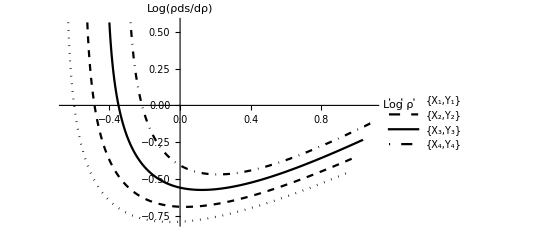

```mathematica
ListLinePlot[{Table[{Log[HP2rho180[s]],Log[.001*HP2rho180[s]/(HP2rho180[s+1]-HP2rho180[s])]},{s,1,921,1}],Table[{Log[HP2rho360[s]],Log[.001*HP2rho360[s]/(HP2rho360[s+1]-HP2rho360[s])]},{s,1,973,1}],Table[{Log[HP2rho540[s]],Log[.001*HP2rho540[s]/(HP2rho540[s+1]-HP2rho540[s])]},{s,1,1038,1}],Table[{Log[HP2rho720[s]],Log[.001*HP2rho720[s]/(HP2rho720[s+1]-HP2rho720[s])]},{s,1,1110,1}]},AxesLabel->{"Log ρ","Log(ρds/dρ)"},PlotStyle->{{Dotted,Black},{Dashed,Black},{Black},{DotDashed,Black}},Ticks->None,PlotLegends->LineLegend[{{{"X_1,Y_1"},{"X_2,Y_2"},{"X_3,Y_3"},{"X_4,Y_4"}}},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5]]
```

LAPSurface

### Set up

```mathematica
kernelcodeCPLAS2="
#define min 0
#define max 1
#define vvv 0
#define uuu 1
#define sign1 -1
#define h 0.001
#define n 1201
#define AlphaLAC (2.0)
#define BetaLASC (2.0)
#define InitRCLAC (1.0)
#define OmegaLASC (1.0)
#define Lambda_Max_LAC (12.718433357775211)
#define ArcLength_Max_LAC (6.764357890136049)
#define Lambda_Min_LAC (12.718433357775211)
#define ArcLength_Min_LAC (6.764357890136049)
#define Lambda_Max_LASC (6.285247558593747)
#define InitRT_Max_LASC (7.303131835937503)
#define ArcLength_Max_LASC (3.1084204465150833)
#define Lambda_Min_LASC (6.285247558593747)
#define InitRT_Min_LASC (7.303131835937503)
#define ArcLength_Min_LASC (3.1084204465150833)
#define Point00x (0.0)
#define Point00y (0.0)
#define Point00z (0.0)
#define Point03x (-0.7077264466498845)
#define Point03y (0.0)
#define Point03z (0.5008767232876717)
#define Point30x (0.0)
#define Point30y (-0.7077264466498845)
#define Point30z (-0.5008767232876717)
#define Point33x (-1.0013149889663)
#define Point33y (-1.0013149889663)
#define Point33z (0.0)

#define maxPoint00x (0.0)
#define maxPoint00y (0.0)
#define maxPoint00z (0.0)
#define maxPoint03x (-0.7077264466498845)
#define maxPoint03y (0.0)
#define maxPoint03z (0.5008767232876717)
#define maxPoint30x (0.0)
#define maxPoint30y (-0.7077264466498845)
#define maxPoint30z (-0.5008767232876717)
#define maxPoint33x (-1.0013149889663)
#define maxPoint33y (-1.0013149889663)
#define maxPoint33z (0.0)


#define ScaleToOrigin_Max_LAC (0.13192365851313362)
#define ScaleToOrigin_Min_LAC (0.13192365851313362)
#define ScaleToOrigin_Max_LASC (0.38164320308766897)
#define ScaleToOrigin_Min_LASC (0.38164320308766897)

#define inidxdu1 ((1-pv)*(maxPoint00x-maxPoint03x)+pv*(maxPoint30x-maxPoint33x)-v1_x1+v2_x1+(1-pv)*u1_t1+pv*u2_t1)
#define inidxdu2 ((1-pv)*(maxPoint00y-maxPoint03y)+pv*(maxPoint30y-maxPoint33y)-v1_x2+v2_x2+(1-pv)*u1_t2+pv*u2_t2)
#define inidxdu3 ((1-pv)*(maxPoint00z-maxPoint03z)+pv*(maxPoint30z-maxPoint33z)-v1_x3+v2_x3+(1-pv)*u1_t3+pv*u2_t3)
#define inidxdv1 ((1-pu)*(maxPoint00x-maxPoint30x)+pu*(maxPoint03x-maxPoint33x)-u1_x1+u2_x1+(1-pu)*v1_t1+pu*v2_t1)
#define inidxdv2 ((1-pu)*(maxPoint00y-maxPoint30y)+pu*(maxPoint03y-maxPoint33y)-u1_x2+u2_x2+(1-pu)*v1_t2+pu*v2_t2)
#define inidxdv3 ((1-pu)*(maxPoint00z-maxPoint30z)+pu*(maxPoint03z-maxPoint33z)-u1_x3+u2_x3+(1-pu)*v1_t3+pu*v2_t3)

#define inid2xdu21 ((1-pv)*u1_dt1+pv*u2_dt1)
#define inid2xdu22 ((1-pv)*u1_dt2+pv*u2_dt2)
#define inid2xdu23 ((1-pv)*u1_dt3+pv*u2_dt3)
#define inid2xdv21 ((1-pu)*v1_dt1+pu*v2_dt1)
#define inid2xdv22 ((1-pu)*v1_dt2+pu*v2_dt2)
#define inid2xdv23 ((1-pu)*v1_dt3+pu*v2_dt3)
#define inid2xdudv1 (-maxPoint00x+maxPoint03x+maxPoint30x-maxPoint33x-u1_t1+u2_t1-v1_t1+v2_t1)
#define inid2xdudv2 (-maxPoint00y+maxPoint03y+maxPoint30y-maxPoint33y-u1_t2+u2_t2-v1_t2+v2_t2)
#define inid2xdudv3 (-maxPoint00z+maxPoint03z+maxPoint30z-maxPoint33z-u1_t3+u2_t3-v1_t3+v2_t3)


#define inid3xdu31 ((1-pv)*u1_d2t1+pv*u2_d2t1)
#define inid3xdu32 ((1-pv)*u1_d2t2+pv*u2_d2t2)
#define inid3xdu33 ((1-pv)*u1_d2t3+pv*u2_d2t3)
#define inid3xdv31 ((1-pu)*v1_d2t1+pu*v2_d2t1)
#define inid3xdv32 ((1-pu)*v1_d2t2+pu*v2_d2t2)
#define inid3xdv33 ((1-pu)*v1_d2t3+pu*v2_d2t3)
#define inid3xdu2dv1 (-u1_dt1+u2_dt1)
#define inid3xdu2dv2 (-u1_dt2+u2_dt2)
#define inid3xdu2dv3 (-u1_dt3+u2_dt3)
#define inid3xdudv21 (-v1_dt1+v2_dt1)
#define inid3xdudv22 (-v1_dt2+v2_dt2)
#define inid3xdudv23 (-v1_dt3+v2_dt3)


#define dxdu1 ((1-pv[i])*(maxPoint00x-maxPoint03x)+pv[i]*(maxPoint30x-maxPoint33x)-v1_x1[i]+v2_x1[i]+(1-pv[i])*u1_t1[i]+pv[i]*u2_t1[i])
#define dxdu2 ((1-pv[i])*(maxPoint00y-maxPoint03y)+pv[i]*(maxPoint30y-maxPoint33y)-v1_x2[i]+v2_x2[i]+(1-pv[i])*u1_t2[i]+pv[i]*u2_t2[i])
#define dxdu3 ((1-pv[i])*(maxPoint00z-maxPoint03z)+pv[i]*(maxPoint30z-maxPoint33z)-v1_x3[i]+v2_x3[i]+(1-pv[i])*u1_t3[i]+pv[i]*u2_t3[i])
#define dxdv1 ((1-pu[i])*(maxPoint00x-maxPoint30x)+pu[i]*(maxPoint03x-maxPoint33x)-u1_x1[i]+u2_x1[i]+(1-pu[i])*v1_t1[i]+pu[i]*v2_t1[i])
#define dxdv2 ((1-pu[i])*(maxPoint00y-maxPoint30y)+pu[i]*(maxPoint03y-maxPoint33y)-u1_x2[i]+u2_x2[i]+(1-pu[i])*v1_t2[i]+pu[i]*v2_t2[i])
#define dxdv3 ((1-pu[i])*(maxPoint00z-maxPoint30z)+pu[i]*(maxPoint03z-maxPoint33z)-u1_x3[i]+u2_x3[i]+(1-pu[i])*v1_t3[i]+pu[i]*v2_t3[i])


#define d2xdu21 ((1-pv[i])*u1_dt1[i]+pv[i]*u2_dt1[i])
#define d2xdu22 ((1-pv[i])*u1_dt2[i]+pv[i]*u2_dt2[i])
#define d2xdu23 ((1-pv[i])*u1_dt3[i]+pv[i]*u2_dt3[i])
#define d2xdv21 ((1-pu[i])*v1_dt1[i]+pu[i]*v2_dt1[i])
#define d2xdv22 ((1-pu[i])*v1_dt2[i]+pu[i]*v2_dt2[i])
#define d2xdv23 ((1-pu[i])*v1_dt3[i]+pu[i]*v2_dt3[i])
#define d2xdudv1 (-maxPoint00x+maxPoint03x+maxPoint30x-maxPoint33x-u1_t1[i]+u2_t1[i]-v1_t1[i]+v2_t1[i])
#define d2xdudv2 (-maxPoint00y+maxPoint03y+maxPoint30y-maxPoint33y-u1_t2[i]+u2_t2[i]-v1_t2[i]+v2_t2[i])
#define d2xdudv3 (-maxPoint00z+maxPoint03z+maxPoint30z-maxPoint33z-u1_t3[i]+u2_t3[i]-v1_t3[i]+v2_t3[i])


#define d3xdu31 ((1-pv[i])*u1_d2t1[i]+pv[i]*u2_d2t1[i])
#define d3xdu32 ((1-pv[i])*u1_d2t2[i]+pv[i]*u2_d2t2[i])
#define d3xdu33 ((1-pv[i])*u1_d2t3[i]+pv[i]*u2_d2t3[i])
#define d3xdv31 ((1-pu[i])*v1_d2t1[i]+pu[i]*v2_d2t1[i])
#define d3xdv32 ((1-pu[i])*v1_d2t2[i]+pu[i]*v2_d2t2[i])
#define d3xdv33 ((1-pu[i])*v1_d2t3[i]+pu[i]*v2_d2t3[i])
#define d3xdu2dv1 (-u1_dt1[i]+u2_dt1[i])
#define d3xdu2dv2 (-u1_dt2[i]+u2_dt2[i])
#define d3xdu2dv3 (-u1_dt3[i]+u2_dt3[i])
#define d3xdudv21 (-v1_dt1[i]+v2_dt1[i])
#define d3xdudv22 (-v1_dt2[i]+v2_dt2[i])
#define d3xdudv23 (-v1_dt3[i]+v2_dt3[i])

#define d4xdu41 ((1-pv[i])*u1_d3t1[i]+pv[i]*u2_d3t1[i])
#define d4xdu42 ((1-pv[i])*u1_d3t2[i]+pv[i]*u2_d3t2[i])
#define d4xdu43 ((1-pv[i])*u1_d3t3[i]+pv[i]*u2_d3t3[i])
#define d4xdv41 ((1-pu[i])*v1_d3t1[i]+pu[i]*v2_d3t1[i])
#define d4xdv42 ((1-pu[i])*v1_d3t2[i]+pu[i]*v2_d3t2[i])
#define d4xdv43 ((1-pu[i])*v1_d3t3[i]+pu[i]*v2_d3t3[i])
#define d4xdu3dv1 (-u1_d2t1[i]+u2_d2t1[i])
#define d4xdu3dv2 (-u1_d2t2[i]+u2_d2t2[i])
#define d4xdu3dv3 (-u1_d2t3[i]+u2_d2t3[i])
#define d4xdudv31 (-v1_d2t1[i]+v2_d2t1[i])
#define d4xdudv32 (-v1_d2t2[i]+v2_d2t2[i])
#define d4xdudv33 (-v1_d2t3[i]+v2_d2t3[i])
#define d4xdu2dv21 (0.0)
#define d4xdu2dv22 (0.0)
#define d4xdu2dv23 (0.0)

#define Coons_x1 ((1-pv[index])*u1_x1[index]+pv[index]*u2_x1[index]+(1-pu[index])*v1_x1[index]+pu[index]*v2_x1[index]-((1-pu[index])*(1-pv[index])*maxPoint00x+pu[index]*(1-pv[index])*maxPoint03x+(1-pu[index])*pv[index]*maxPoint30x+pu[index]*pv[index]*maxPoint33x))
#define Coons_x2 ((1-pv[index])*u1_x2[index]+pv[index]*u2_x2[index]+(1-pu[index])*v1_x2[index]+pu[index]*v2_x2[index]-((1-pu[index])*(1-pv[index])*maxPoint00y+pu[index]*(1-pv[index])*maxPoint03y+(1-pu[index])*pv[index]*maxPoint30y+pu[index]*pv[index]*maxPoint33y))
#define Coons_x3 ((1-pv[index])*u1_x3[index]+pv[index]*u2_x3[index]+(1-pu[index])*v1_x3[index]+pu[index]*v2_x3[index]-((1-pu[index])*(1-pv[index])*maxPoint00z+pu[index]*(1-pv[index])*maxPoint03z+(1-pu[index])*pv[index]*maxPoint30z+pu[index]*pv[index]*maxPoint33z))


#define repiniSurNorvec iniSurNorvec(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,normv_C)
#define repiniDSurNvDu iniDSurNvDu(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,dnormvdu_C)
#define repiniDSurNvDv iniDSurNvDv(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,dnormvdv_C)
#define repiniScalarSurNor iniScalarSurNor(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,Scal)
#define repinicoefE inicoefE(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repiniDEDu iniDEDu(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniDEDv iniDEDv(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repinicoefF inicoefF(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repiniDFDu iniDFDu(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniDFDv iniDFDv(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repinicoefG inicoefG(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repiniDGDu iniDGDu(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniDGDv iniDGDv(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repinicoefL inicoefL(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repinicoefM inicoefM(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repinicoefN inicoefN(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniGaussCurva iniGaussCurva(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniMeanCurva iniMeanCurva(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniMaxPrinci iniMaxPrinci(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniMinPrinci iniMinPrinci(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniPrinci iniPrinci(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)

#define repiniDcoefL_2 iniDcoefL_2(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,CoeffL)
#define repiniDcoefM_2 iniDcoefM_2(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,CoeffM)
#define repiniDcoefN_2 iniDcoefN_2(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,CoeffN)
#define repiniDGaussCurva_2 iniDGaussCurva_2(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,GCurva)
#define repiniDMeanCurva_2 iniDMeanCurva_2(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,MCurva)
#define repiniDPrinci_2 iniDPrinci_2(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,optimum,PCurva)
#define repiniEta iniEta(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniMiu  iniMiu(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDuDs iniDuDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDvDs iniDvDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDEDs iniDEDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDFDs iniDFDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDGDs iniDGDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDLDs iniDLDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,optimum)
#define repiniDMDs iniDMDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,optimum)
#define repiniDNDs iniDNDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,optimum)
#define repiniDPrinciDs iniDPrinciDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,optimum)
#define repiniDvDt iniDvDt(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDuDt iniDuDt(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDSurDs iniDSurDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum,tangv)
#define repiniSurNor iniSurNor(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,Snor_C)
#define repiniBinormalSur iniBinormalSur(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum,binormv_C)
#define repiniAlp1 iniAlp1(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum,Alp1_C)
#define repiniBeta1 iniBeta1(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,optimum)

#define repSurNorvec SurNorvec(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,normv_C)
#define repDSurNvDu DSurNvDu(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,dnormvdu_C)
#define repDSurNvDv DSurNvDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,dnormvdv_C)
#define repD2SurNvDu2 D2SurNvDu2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,d2normvdu2_C)
#define repD2SurNvDuDv D2SurNvDuDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,d2normvdudv_C)
#define repD2SurNvDv2 D2SurNvDv2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,d2normvdv2_C)
#define repScalarSurNor ScalarSurNor(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,Scal)
#define repcoefE coefE(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repDEDu DEDu(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repDEDv DEDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repD2EDu2 D2EDu2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2EDuDv D2EDuDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2EDv2 D2EDv2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repcoefF coefF(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repDFDu DFDu(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repDFDv DFDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repD2FDu2 D2FDu2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2FDuDv D2FDuDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2FDv2 D2FDv2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repcoefG coefG(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repDGDu DGDu(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repDGDv DGDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repD2GDu2 D2GDu2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2GDuDv D2GDuDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2GDv2 D2GDv2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repcoefL coefL(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repcoefM coefM(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repcoefN coefN(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repGaussCurva GaussCurva(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repMeanCurva MeanCurva(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repMaxPrinci MaxPrinci(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repMinPrinci MinPrinci(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repPrinci Princi(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDcoefL_2 DcoefL_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,CoeffL)
#define repDcoefM_2 DcoefM_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,CoeffM)
#define repDcoefN_2 DcoefN_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,CoeffN)
#define repDGaussCurva_2 DGaussCurva_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,GCurva)
#define repDMeanCurva_2 DMeanCurva_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,MCurva)
#define repDPrinci_2 DPrinci_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum,PCurva)
#define repEta Eta(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repMiu  Miu(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDuDs DuDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDvDs DvDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDEDs DEDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDFDs DFDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDGDs DGDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDLDs DLDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repDMDs DMDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repDNDs DNDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repDPrinciDs DPrinciDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repDvDt DvDt(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDuDt DuDt(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDSurDs DSurDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum,tangv)
#define repSurNor SurNor(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,Snor_C)
#define repBinormalSur BinormalSur(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum,binormv_C)
#define repAlp1 Alp1(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum,Alp1_C)
#define repBeta1 Beta1(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)

#define repCurvecurvature Curvecurvature(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,D2uDs2,D2vDs2,GeoCur,optimum)
#define repD2EDs2 D2EDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,D2uDs2,D2vDs2,GeoCur,optimum)
#define repD2FDs2 D2FDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,D2uDs2,D2vDs2,GeoCur,optimum)
#define repD2GDs2 D2GDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,D2uDs2,D2vDs2,GeoCur,optimum)
#define repD2LDs2 D2LDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,D2uDs2,D2vDs2,GeoCur,optimum)
#define repD2MDs2 D2MDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,D2uDs2,D2vDs2,GeoCur,optimum)
#define repD2NDs2 D2NDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,D2uDs2,D2vDs2,GeoCur,optimum)
#define repD2PrinciDs2 D2PrinciDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,D2uDs2,D2vDs2,GeoCur,optimum)
#define repD2SurDs2 D2SurDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,D2uDs2,D2vDs2,GeoCur,optimum,dtangds)
#define repCurvenormaloS CurvenormaloS(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,D2uDs2,D2vDs2,GeoCur,optimum,norv)
#define repCurvebinormaloS CurvebinormaloS(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,D2uDs2,D2vDs2,GeoCur,optimum,binorv)
#define repAlp2 Alp2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,D2uDs2,D2vDs2,GeoCur,optimum,Alp2_C)
#define repBeta2 Beta2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,D2uDs2,D2vDs2,GeoCur,optimum)





#define opt1 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float normv_C[])
#define opt2 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3)
#define opt3 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3)
#define opt4 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,mint optimum)
 #define opt5 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,mint optimum,float tangv_C[])
#define opt6 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,float dnormv_C[])
#define opt7 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,float Scal[])
#define opt8 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u1_d2t1,float u1_d2t2,float u1_d2t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float u2_d2t1,float u2_d2t2,float u2_d2t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v1_d2t1,float v1_d2t2,float v1_d2t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,float v2_d2t1,float v2_d2t2,float v2_d2t3,float coeff[])
#define opt9 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u1_d2t1,float u1_d2t2,float u1_d2t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float u2_d2t1,float u2_d2t2,float u2_d2t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v1_d2t1,float v1_d2t2,float v1_d2t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,float v2_d2t1,float v2_d2t2,float v2_d2t3,mint optimum,float coeff[])
#define opt10 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u1_d2t1,float u1_d2t2,float u1_d2t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float u2_d2t1,float u2_d2t2,float u2_d2t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v1_d2t1,float v1_d2t2,float v1_d2t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,float v2_d2t1,float v2_d2t2,float v2_d2t3,mint optimum)

#define opt11 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,mint optimum,float Alph_C[])
#define opt12 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float Snor_C[])
#define opt13 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,mint optimum,float binormv_C[])
#define opt14 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u1_d2t1,float u1_d2t2,float u1_d2t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float u2_d2t1,float u2_d2t2,float u2_d2t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v1_d2t1,float v1_d2t2,float v1_d2t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,float v2_d2t1,float v2_d2t2,float v2_d2t3,mint optimum,float x[])

#define opt15 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float normv_C[]) 
#define opt16 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[])
#define opt17 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[])
#define opt18 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],mint optimum)
#define opt19 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],mint optimum,float tangv_C[])
#define opt20 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float dnormv_C[])
#define opt21 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float d2normv_C[])
#define opt22 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float Scal[])
#define opt23 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[])
#define opt24 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u1_d3t1[],float u1_d3t2[],float u1_d3t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float u2_d3t1[],float u2_d3t2[],float u2_d3t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v1_d3t1[],float v1_d3t2[],float v1_d3t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float v2_d3t1[],float v2_d3t2[],float v2_d3t3[],float coeff[])
#define opt25 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u1_d3t1[],float u1_d3t2[],float u1_d3t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float u2_d3t1[],float u2_d3t2[],float u2_d3t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v1_d3t1[],float v1_d3t2[],float v1_d3t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float v2_d3t1[],float v2_d3t2[],float v2_d3t3[],mint optimum,float coeff[])
#define opt26 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u1_d3t1[],float u1_d3t2[],float u1_d3t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float u2_d3t1[],float u2_d3t2[],float u2_d3t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v1_d3t1[],float v1_d3t2[],float v1_d3t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float v2_d3t1[],float v2_d3t2[],float v2_d3t3[],mint optimum)
#define opt27 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u1_d3t1[],float u1_d3t2[],float u1_d3t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float u2_d3t1[],float u2_d3t2[],float u2_d3t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v1_d3t1[],float v1_d3t2[],float v1_d3t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float v2_d3t1[],float v2_d3t2[],float v2_d3t3[],float D2uDs2[],float D2vDs2[],float GeoCur[],mint optimum)
#define opt28 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u1_d3t1[],float u1_d3t2[],float u1_d3t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float u2_d3t1[],float u2_d3t2[],float u2_d3t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v1_d3t1[],float v1_d3t2[],float v1_d3t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float v2_d3t1[],float v2_d3t2[],float v2_d3t3[],float D2uDs2[],float D2vDs2[],float GeoCur[],mint optimum,float coeff[])


__device__ float inicurvature_LAC(float t,float Alpha,float Lambda,float InitRC,float Total_s) 
{
if(Alpha==-1)
	{return ((float) 1)/InitRC-Lambda*t*Total_s;}
else if(Alpha==0) 
	{return ((float) 1)/exp(Lambda*t*Total_s+log(InitRC));} 
else if(Alpha==1)
	{return ((float) 1)/(InitRC+Lambda*t*Total_s);}
else if(Alpha==2)
	{return ((float) 1)/sqrt(pow(InitRC,2)+2.0*Lambda*t*Total_s);}
else
	{return pow(pow(InitRC,Alpha)+Lambda*Alpha*t*Total_s,-((float) 1)/Alpha);}
}

__device__ float inidcLACdx(float t,float Alpha,float Lambda,float InitRC,float Total_s) 
{
if(Alpha==-1)
	{return -Total_s*Lambda;}
else if(Alpha==0) 
	{return -Total_s*(Lambda*exp(-Lambda*t*Total_s))/InitRC;} 
else if(Alpha==1)
	{return -Total_s*Lambda/pow(InitRC+Lambda*t*Total_s,2);}
else if(Alpha==2)
	{return -Total_s*Lambda/((pow(InitRC,2)+2.0*Lambda*t*Total_s)*sqrt(pow(InitRC,2)+2.0*Lambda*t*Total_s));}
else
	{return -Total_s*Lambda*pow(pow(InitRC,Alpha)+Lambda*Alpha*t*Total_s,-((float) 1)-((float) 1)/Alpha);}
}
__device__ float inid2cLACdx2(float t,float Alpha,float Lambda,float InitRC,float Total_s) 
{
if(Alpha==-1)
	{return 0;}
else if(Alpha==0) 
	{return pow(Total_s,2)*(pow(Lambda,2)*exp(-Lambda*t*Total_s))/InitRC;} 
else if(Alpha==1)
	{return pow(Total_s,2)*((float) 2)*pow(Lambda,2)/pow(InitRC+Lambda*t*Total_s,3);}
else if(Alpha==2)
	{return 3.0*pow(Total_s,2)*pow(Lambda,2)/(pow(pow(InitRC,2)+2.0*Lambda*t*Total_s,2)*(sqrt(pow(InitRC,2)+2.0*Lambda*t*Total_s)));}
else
	{return (((float) 1)+Alpha)*pow(Total_s,2)*pow(Lambda,2)*pow(pow(InitRC,Alpha)+Lambda*Alpha*t*Total_s,-((float) 2)-((float) 1)/Alpha);}
}

__device__ float iniTorsion_LASC(float t,float Beta,float Omega,float InitRT,float Total_s) 
{
if(Beta==-1)
	{return ((float) 1)/InitRT-Omega*t*Total_s;}
else if(Beta==0) 
	{return ((float) 1)/exp(Omega*t*Total_s+log(InitRT));} 
else if(Beta==1)
	{return ((float) 1)/(InitRT+Omega*t*Total_s);}
else if(Beta==2)
	{return ((float) 1)/sqrt(pow(InitRT,2)+2.0*Omega*t*Total_s);}
else
	{return pow(pow(InitRT,Beta)+Omega*Beta*t*Total_s,-((float) 1)/Beta);}
}

__device__ float inidtLASCdx(float t,float Beta,float Omega,float InitRT,float Total_s) 
{
if(Beta==-1)
	{return -Total_s*Omega;}
else if(Beta==0) 
	{return -Total_s*(Omega*exp(-Omega*t*Total_s))/InitRT;} 
else if(Beta==1)
	{return -Total_s*Omega/pow(InitRT+Omega*t*Total_s,2);}
else if(Beta==2)
	{return -Total_s*Omega/((pow(InitRT,2)+2.0*Omega*t*Total_s)*sqrt(pow(InitRT,2)+2.0*Omega*t*Total_s));}
else
	{return -Total_s*Omega*pow(pow(InitRT,Beta)+Omega*Beta*t*Total_s,-((float) 1)-((float) 1)/Beta);}
}

__device__ float inid2tLASCdx2(float t,float Beta,float Omega,float InitRT,float Total_s) 
{
if(Beta==-1)
	{return 0;}
else if(Beta==0) 
	{return pow(Total_s,2)*(pow(Omega,2)*exp(-Omega*t*Total_s))/InitRT;} 
else if(Beta==1)
	{return pow(Total_s,2)*((float) 2)*pow(Omega,2)/pow(InitRT+Omega*t*Total_s,3);}
else if(Beta==2)
	{return pow(Total_s,2)*(((float) 3)*pow(Omega,2))/sqrt(pow(pow(InitRT,2)+((float) 2)*Omega*t*Total_s,5));}
else
	{return (((float) 1)+Beta)*pow(Total_s,2)*pow(Omega,2)*pow(pow(InitRT,Beta)+Omega*Beta*t*Total_s,-((float) 2)-((float) 1)/Beta);}
}


__device__ void iniSurNorvec opt1 
{
	normv_C[0] =inidxdu2*inidxdv3-inidxdu3*inidxdv2; 
	normv_C[1] =inidxdu3*inidxdv1-inidxdu1*inidxdv3;
	normv_C[2] =inidxdu1*inidxdv2-inidxdu2*inidxdv1; 
}
__device__ void iniDSurNvDu opt6
{
	dnormv_C[0] =(inid2xdu22*inidxdv3-inid2xdu23*inidxdv2)+(inidxdu2*inid2xdudv3-inidxdu3*inid2xdudv2); 
	dnormv_C[1] =(inid2xdu23*inidxdv1-inid2xdu21*inidxdv3)+(inidxdu3*inid2xdudv1-inidxdu1*inid2xdudv3);
	dnormv_C[2] =(inid2xdu21*inidxdv2-inid2xdu22*inidxdv1)+(inidxdu1*inid2xdudv2-inidxdu2*inid2xdudv1); 
}
__device__ void iniDSurNvDv opt6
{
	dnormv_C[0] =(inid2xdudv2*inidxdv3-inid2xdudv3*inidxdv2)+(inidxdu2*inid2xdv23-inidxdu3*inid2xdv22); 
	dnormv_C[1] =(inid2xdudv3*inidxdv1-inid2xdudv1*inidxdv3)+(inidxdu3*inid2xdv21-inidxdu1*inid2xdv23); 
	dnormv_C[2] =(inid2xdudv1*inidxdv2-inid2xdudv2*inidxdv1)+(inidxdu1*inid2xdv22-inidxdu2*inid2xdv21); 
}

__device__ void iniScalarSurNor opt7
{
float ScalSNor,DScalSNorDu,DScalSNorDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];

repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;


ScalSNor = sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
DScalSNorDu = (normv_C[0]*dnormvdu_C[0]+normv_C[1]*dnormvdu_C[1]+normv_C[2]*dnormvdu_C[2])/ScalSNor;
DScalSNorDv = (normv_C[0]*dnormvdv_C[0]+normv_C[1]*dnormvdv_C[1]+normv_C[2]*dnormvdv_C[2])/ScalSNor;


Scal[0] = ScalSNor;
Scal[1] = DScalSNorDu;
Scal[2] = DScalSNorDv;
}

__device__ float inicoefE opt2
{
	return inidxdu1*inidxdu1+inidxdu2*inidxdu2+inidxdu3*inidxdu3; 
}
__device__ float iniDEDu opt3
{
	return 2.0*(inidxdu1*inid2xdu21+inidxdu2*inid2xdu22+inidxdu3*inid2xdu23);
}
__device__ float iniDEDv opt3
{
	return 2.0*(inidxdu1*inid2xdudv1+inidxdu2*inid2xdudv2+inidxdu3*inid2xdudv3);
}

 
__device__ float inicoefF opt2
{ 
	return (inidxdu1*inidxdv1+inidxdu2*inidxdv2+inidxdu3*inidxdv3); 
}
__device__ float iniDFDu opt3
{ 
	return inidxdv1*inid2xdu21+inidxdv2*inid2xdu22+inidxdv3*inid2xdu23 + inidxdu1*inid2xdudv1+inidxdu2*inid2xdudv2+inidxdu3*inid2xdudv3;
}
__device__ float iniDFDv opt3
{ 
	return inidxdv1*inid2xdudv1+inidxdv2*inid2xdudv2+inidxdv3*inid2xdudv3 + inidxdu1*inid2xdv21+inidxdu2*inid2xdv22+inidxdu3*inid2xdv23;
}

__device__ float inicoefG opt2
{ 
	return inidxdv1*inidxdv1+inidxdv2*inidxdv2+inidxdv3*inidxdv3; 
}
__device__ float iniDGDu opt3
{ 
	return 2.0*(inidxdv1*inid2xdudv1+inidxdv2*inid2xdudv2+inidxdv3*inid2xdudv3);
}
__device__ float iniDGDv opt3
{ 
	return 2.0*(inidxdv1*inid2xdv21+inidxdv2*inid2xdv22+inidxdv3*inid2xdv23);
}

__device__ float inicoefL opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdu21+normv_C[1]*inid2xdu22+normv_C[2]*inid2xdu23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float inicoefM opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdudv1+normv_C[1]*inid2xdudv2+normv_C[2]*inid2xdudv3)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float inicoefN opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdv21+normv_C[1]*inid2xdv22+normv_C[2]*inid2xdv23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float iniGaussCurva opt3
{
	return (repinicoefL*repinicoefN-pow(repinicoefM,2))/(repinicoefE*repinicoefG-pow(repinicoefF,2)); 
}
__device__ float iniMeanCurva opt3
{
	return 0.5*(repinicoefE*repinicoefN+repinicoefG*repinicoefL-2*repinicoefF*repinicoefM)/(repinicoefE*repinicoefG-pow(repinicoefF,2));
}
__device__ float iniMaxPrinci opt3
{
	return repiniMeanCurva+sqrt(pow(repiniMeanCurva,2)-repiniGaussCurva); 
}

__device__ float iniMinPrinci opt3
{
	return repiniMeanCurva-sqrt(pow(repiniMeanCurva,2)-repiniGaussCurva); 
}
__device__ float iniPrinci opt4
{ 	
	if(optimum==max) 
	{return repiniMaxPrinci;} 
	else if(optimum==min)
	{return repiniMinPrinci;}
	else
	{return 0;}
}
__device__ void iniDcoefL_2 opt8
{

float CoeL,DCoeLDu,DCoeLDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];

repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;
repiniScalarSurNor;

CoeL = (normv_C[0]*inid2xdu21+normv_C[1]*inid2xdu22+normv_C[2]*inid2xdu23)/Scal[0];
DCoeLDu = ((dnormvdu_C[0]*inid2xdu21+dnormvdu_C[1]*inid2xdu22+dnormvdu_C[2]*inid2xdu23)+(normv_C[0]*inid3xdu31+normv_C[1]*inid3xdu32+normv_C[2]*inid3xdu33)-Scal[1]*CoeL)/Scal[0];
DCoeLDv = ((dnormvdv_C[0]*inid2xdu21+dnormvdv_C[1]*inid2xdu22+dnormvdv_C[2]*inid2xdu23)+(normv_C[0]*inid3xdu2dv1+normv_C[1]*inid3xdu2dv2+normv_C[2]*inid3xdu2dv3)-Scal[2]*CoeL)/Scal[0];

coeff[0] = CoeL;
coeff[1] = DCoeLDu;
coeff[2] = DCoeLDv;

}
__device__ void iniDcoefM_2 opt8
{
float CoeM,DCoeMDu,DCoeMDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];
repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;
repiniScalarSurNor;

CoeM = (normv_C[0]*inid2xdudv1+normv_C[1]*inid2xdudv2+normv_C[2]*inid2xdudv3)/Scal[0];
DCoeMDu = ((dnormvdu_C[0]*inid2xdudv1+dnormvdu_C[1]*inid2xdudv2+dnormvdu_C[2]*inid2xdudv3)+(normv_C[0]*inid3xdu2dv1+normv_C[1]*inid3xdu2dv2+normv_C[2]*inid3xdu2dv3)-Scal[1]*CoeM)/Scal[0];
DCoeMDv = ((dnormvdv_C[0]*inid2xdudv1+dnormvdv_C[1]*inid2xdudv2+dnormvdv_C[2]*inid2xdudv3)+(normv_C[0]*inid3xdudv21+normv_C[1]*inid3xdudv22+normv_C[2]*inid3xdudv23)-Scal[2]*CoeM)/Scal[0];


coeff[0] = CoeM;
coeff[1] = DCoeMDu;
coeff[2] = DCoeMDv;
}
__device__ void iniDcoefN_2 opt8
{
float CoeN,DCoeNDu,DCoeNDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];
repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;
repiniScalarSurNor;

CoeN = (normv_C[0]*inid2xdv21+normv_C[1]*inid2xdv22+normv_C[2]*inid2xdv23)/Scal[0];
DCoeNDu = ((dnormvdu_C[0]*inid2xdv21+dnormvdu_C[1]*inid2xdv22+dnormvdu_C[2]*inid2xdv23)+(normv_C[0]*inid3xdudv21+normv_C[1]*inid3xdudv22+normv_C[2]*inid3xdudv23)-Scal[1]*CoeN)/Scal[0];
DCoeNDv = ((dnormvdv_C[0]*inid2xdv21+dnormvdv_C[1]*inid2xdv22+dnormvdv_C[2]*inid2xdv23)+(normv_C[0]*inid3xdv31+normv_C[1]*inid3xdv32+normv_C[2]*inid3xdv33)-Scal[2]*CoeN)/Scal[0];

coeff[0] = CoeN;
coeff[1] = DCoeNDu;
coeff[2] = DCoeNDv;

}
__device__ void iniDGaussCurva_2 opt8 
{
float GCurv,DGCurvDu,DGCurvDv;
float CoeffL[3];
float CoeffM[3];
float CoeffN[3];
repiniDcoefL_2;
repiniDcoefM_2;
repiniDcoefN_2;

GCurv= (CoeffL[0]*CoeffN[0]-pow(CoeffM[0],2))/(repinicoefE*repinicoefG-pow(repinicoefF,2));
DGCurvDu = ((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repinicoefG*repiniDEDu-2*repinicoefF*repiniDFDu+repinicoefE*repiniDGDu)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*CoeffL[1]-2*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));
DGCurvDv =((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repinicoefG*repiniDEDv-2*repinicoefF*repiniDFDv+repinicoefE*repiniDGDv)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*CoeffL[2]-2*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));


coeff[0] = GCurv;
coeff[1] = DGCurvDu;
coeff[2] = DGCurvDv;

}
__device__ void iniDMeanCurva_2 opt8
{
float MCurv,DMCurvDu,DMCurvDv;
float CoeffL[3];
float CoeffM[3];
float CoeffN[3];
repiniDcoefL_2;
repiniDcoefM_2;
repiniDcoefN_2;

MCurv = 0.5*(repinicoefE*CoeffN[0]+repinicoefG*CoeffL[0]-2*repinicoefF*CoeffM[0])/(repinicoefE*repinicoefG-pow(repinicoefF,2));
DMCurvDu = 0.5*(-(repinicoefG*CoeffL[0]-2*repinicoefF*CoeffM[0]+repinicoefE*CoeffN[0])*(repinicoefG*repiniDEDu-2*repinicoefF*repiniDFDu+repinicoefE*repiniDGDu)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*repiniDEDu-2*CoeffM[0]*repiniDFDu+CoeffL[0]*repiniDGDu+repinicoefG*CoeffL[1]-2*repinicoefF*CoeffM[1]+repinicoefE*CoeffN[1]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));
DMCurvDv = 0.5*(-(repinicoefG*CoeffL[0]-2*repinicoefF*CoeffM[0]+repinicoefE*CoeffN[0])*(repinicoefG*repiniDEDv-2*repinicoefF*repiniDFDv+repinicoefE*repiniDGDv)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*repiniDEDv-2*CoeffM[0]*repiniDFDv+CoeffL[0]*repiniDGDv+repinicoefG*CoeffL[2]-2*repinicoefF*CoeffM[2]+repinicoefE*CoeffN[2]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));



coeff[0] = MCurv;
coeff[1] = DMCurvDu;
coeff[2] = DMCurvDv;
}
__device__ void iniDPrinci_2 opt9
{
float Princip,DPrincipDu,DPrincipDv;
float GCurva[3];
float MCurva[3];
repiniDGaussCurva_2;
repiniDMeanCurva_2;

if(optimum==max) 
{Princip = MCurva[0]+sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]+(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]+(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));

}
else if(optimum==min)
{Princip = MCurva[0]-sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]-(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]-(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));

}
else
{Princip = 0;
DPrincipDu = 0;
DPrincipDv = 0;
}

coeff[0] = Princip;
coeff[1] = DPrincipDu;
coeff[2] = DPrincipDv;

}

__device__ float iniEta opt4
{
	return sign1/sqrt(repinicoefE*pow(repinicoefM-repiniPrinci*repinicoefF,2)-2*repinicoefF*(repinicoefM-repiniPrinci*repinicoefF)*(repinicoefL-repiniPrinci*repinicoefE)+repinicoefG*pow(repinicoefL-repiniPrinci*repinicoefE,2));
}
__device__ float iniMiu opt4
{
	return sign1/sqrt(repinicoefE*pow(repinicoefN-repiniPrinci*repinicoefG,2)-2*repinicoefF*(repinicoefM-repiniPrinci*repinicoefF)*(repinicoefN-repiniPrinci*repinicoefG)+repinicoefG*pow(repinicoefM-repiniPrinci*repinicoefF,2));
}
__device__ float iniDuDs opt4
{ 
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return repiniEta*(repinicoefM-repiniPrinci*repinicoefF);}
else
	{return repiniMiu*(repinicoefN-repiniPrinci*repinicoefG);}
}
__device__ float iniDvDs opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return -repiniEta*(repinicoefL-repiniPrinci*repinicoefE);}
else
	{return -repiniMiu*(repinicoefM-repiniPrinci*repinicoefF);}
}


__device__ float iniDEDs opt4
{
	return repiniDEDu*repiniDuDs+repiniDEDv*repiniDvDs;
}
__device__ float iniDFDs opt4
{
	return repiniDFDu*repiniDuDs+repiniDFDv*repiniDvDs;
}
__device__ float iniDGDs opt4
{
	return repiniDGDu*repiniDuDs+repiniDGDv*repiniDvDs;
}
__device__ float iniDLDs opt10
{
float CoeffL[3];
repiniDcoefL_2;

	return CoeffL[1]*repiniDuDs+CoeffL[2]*repiniDvDs;
}
__device__ float iniDMDs opt10
{
float CoeffM[3];
repiniDcoefM_2;

	return CoeffM[1]*repiniDuDs+CoeffM[2]*repiniDvDs;
}
__device__ float iniDNDs opt10
{
float CoeffN[3];
repiniDcoefN_2;

	return CoeffN[1]*repiniDuDs+CoeffN[2]*repiniDvDs;
}
__device__ float iniDPrinciDs opt10
{
float PCurva[3];
repiniDPrinci_2;

	return PCurva[1]*repiniDuDs+PCurva[2]*repiniDvDs;
}
__device__ float iniDuDt opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return (repinicoefM-repiniPrinci*repinicoefF);}
else
	{return (repinicoefN-repiniPrinci*repinicoefG);}
}
__device__ float iniDvDt opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return (repinicoefL-repiniPrinci*repinicoefE);}
else
	{return (repinicoefM-repiniPrinci*repinicoefF);}
}
__device__ void iniDSurDs opt5
{
	tangv_C[0] =inidxdu1*repiniDuDs+inidxdv1*repiniDvDs;
	tangv_C[1] =inidxdu2*repiniDuDs+inidxdv2*repiniDvDs;
	tangv_C[2] =inidxdu3*repiniDuDs+inidxdv3*repiniDvDs;
}

__device__ void iniAlp1 opt11
{
	Alph_C[0]=(inid2xdu21*pow(repiniDuDs,2)+2*inid2xdudv1*repiniDuDs*repiniDvDs+inid2xdv21*pow(repiniDvDs,2));
	Alph_C[1]=(inid2xdu22*pow(repiniDuDs,2)+2*inid2xdudv2*repiniDuDs*repiniDvDs+inid2xdv22*pow(repiniDvDs,2));
	Alph_C[2]=(inid2xdu23*pow(repiniDuDs,2)+2*inid2xdudv3*repiniDuDs*repiniDvDs+inid2xdv23*pow(repiniDvDs,2));
}
__device__ void iniSurNor opt12 
{
	float normv_C[3];
	repiniSurNorvec;
	Snor_C[0] =normv_C[0]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]); 
	Snor_C[1] =normv_C[1]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
	Snor_C[2] =normv_C[2]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]); 
}

__device__ void iniBinormalSur opt13
{
	float Snor_C[3];
	float tangv[3];
	repiniSurNor;
	repiniDSurDs;

	binormv_C[0] =Snor_C[1]*tangv[2] -Snor_C[2]*tangv[1];
	binormv_C[1] =Snor_C[2]*tangv[0] -Snor_C[0]*tangv[2];
	binormv_C[2] =Snor_C[0]*tangv[1] -Snor_C[1]*tangv[0];
}
__device__ float iniBeta1 opt10
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return (-(repiniDLDs-repiniDPrinciDs*repinicoefE-repiniPrinci*repiniDEDs)*repiniDuDs-(repiniDMDs-repiniDPrinciDs*repinicoefF-repiniPrinci*repiniDFDs)*repiniDvDs);}
else
	{return (-(repiniDMDs-repiniDPrinciDs*repinicoefF-repiniPrinci*repiniDFDs)*repiniDuDs-(repiniDNDs-repiniDPrinciDs*repinicoefG-repiniPrinci*repiniDGDs)*repiniDvDs);}
}

__device__ void LUDecomposition3x3 opt14
{
	mint rc=3;
	float binormv_C[3];
	float Alp1_C[3];
	repiniBinormalSur;
	repiniAlp1;
	float matrixA[3][3]={
	{repinicoefE,repinicoefF,-(binormv_C[0]*inidxdu1+binormv_C[1]*inidxdu2+binormv_C[2]*inidxdu3)},
	{repinicoefF,repinicoefG,-(binormv_C[0]*inidxdv1+binormv_C[1]*inidxdv2+binormv_C[2]*inidxdv3)},
	{repiniDvDt,repiniDuDt,0}};

	float matrixB[3]={-(Alp1_C[0]*inidxdu1+Alp1_C[1]*inidxdu2+Alp1_C[2]*inidxdu3),-(Alp1_C[0]*inidxdv1+Alp1_C[1]*inidxdv2+Alp1_C[2]*inidxdv3),repiniBeta1};
	float Lower[3][3];
	float Upper[3][3];
	float y[3];
	float sum;
	for(mint ii=0; ii<rc; ii++)
			{
				for(mint jj=0; jj<rc; jj++)
				{
					sum = 0;
					if(ii==jj)
					{
					Lower[ii][jj]=1;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else if(ii < jj) 
					{
					Lower[ii][jj]=0;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else 
					{
					Upper[ii][jj]=0;
					for (mint kk = 0; kk < jj; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Lower[ii][jj] =(matrixA[ii][jj] - sum)/Upper[jj][jj];
					}
				}
			}
	for (mint ii = 0; ii < rc; ii++)
	{
		sum = 0;
		for (mint jj = 0; jj < ii; jj++)
			{sum += Lower[ii][jj] * y[jj];}
		y[ii] = matrixB[ii] - sum;
	}
	for (mint ii = rc - 1; ii >= 0; ii--)
	{
		sum = 0;
		for (mint jj = ii + 1; jj < rc; jj++)
			{sum += Upper[ii][jj] * x[jj];}
		x[ii] = (y[ii] - sum)/Upper[ii][ii];
	}
}

__device__ void SurNorvec opt15 
{
	normv_C[0] =dxdu2*dxdv3-dxdu3*dxdv2; 
	normv_C[1] =dxdu3*dxdv1-dxdu1*dxdv3;
	normv_C[2] =dxdu1*dxdv2-dxdu2*dxdv1; 
}
__device__ void DSurNvDu opt20
{
	dnormv_C[0] =(d2xdu22*dxdv3-d2xdu23*dxdv2)+(dxdu2*d2xdudv3-dxdu3*d2xdudv2); 
	dnormv_C[1] =(d2xdu23*dxdv1-d2xdu21*dxdv3)+(dxdu3*d2xdudv1-dxdu1*d2xdudv3);
	dnormv_C[2] =(d2xdu21*dxdv2-d2xdu22*dxdv1)+(dxdu1*d2xdudv2-dxdu2*d2xdudv1); 
}
__device__ void DSurNvDv opt20
{
	dnormv_C[0] =(d2xdudv2*dxdv3-d2xdudv3*dxdv2)+(dxdu2*d2xdv23-dxdu3*d2xdv22); 
	dnormv_C[1] =(d2xdudv3*dxdv1-d2xdudv1*dxdv3)+(dxdu3*d2xdv21-dxdu1*d2xdv23); 
	dnormv_C[2] =(d2xdudv1*dxdv2-d2xdudv2*dxdv1)+(dxdu1*d2xdv22-dxdu2*d2xdv21); 
}
__device__ void D2SurNvDu2 opt21
{
	d2normv_C[0] =(d3xdu32*dxdv3-d3xdu33*dxdv2)+2.0*(d2xdu22*d2xdudv3-d2xdu23*d2xdudv2)+(dxdu2*d3xdu2dv3-dxdu3*d3xdu2dv2); 
	d2normv_C[1] =(d3xdu33*dxdv1-d3xdu31*dxdv3)+2.0*(d2xdu23*d2xdudv1-d2xdu21*d2xdudv3)+(dxdu3*d3xdu2dv1-dxdu1*d3xdu2dv3); 
	d2normv_C[2] =(d3xdu31*dxdv2-d3xdu32*dxdv1)+2.0*(d2xdu21*d2xdudv2-d2xdu22*d2xdudv1)+(dxdu1*d3xdu2dv2-dxdu2*d3xdu2dv1); 
}
__device__ void D2SurNvDuDv opt21
{
	d2normv_C[0] =(d3xdu2dv2*dxdv3-d3xdu2dv3*dxdv2)+(d2xdu22*d2xdv23-d2xdu23*d2xdv22)+(dxdu2*d3xdudv23-dxdu3*d3xdudv22); 
	d2normv_C[1] =(d3xdu2dv3*dxdv1-d3xdu2dv1*dxdv3)+(d2xdu23*d2xdv21-d2xdu21*d2xdv23)+(dxdu3*d3xdudv21-dxdu1*d3xdudv23); 
	d2normv_C[2] =(d3xdu2dv1*dxdv2-d3xdu2dv2*dxdv1)+(d2xdu21*d2xdv22-d2xdu22*d2xdv21)+(dxdu1*d3xdudv22-dxdu2*d3xdudv21); 
}
__device__ void D2SurNvDv2 opt21
{
	d2normv_C[0] =(d3xdudv22*dxdv3-d3xdudv23*dxdv2)+2.0*(d2xdudv2*d2xdv23-d2xdudv3*d2xdv22)+(dxdu2*d3xdv33-dxdu3*d3xdv32); 
	d2normv_C[1] =(d3xdudv23*dxdv1-d3xdudv21*dxdv3)+2.0*(d2xdudv3*d2xdv21-d2xdudv1*d2xdv23)+(dxdu3*d3xdv31-dxdu1*d3xdv33); 
	d2normv_C[2] =(d3xdudv21*dxdv2-d3xdudv22*dxdv1)+2.0*(d2xdudv1*d2xdv22-d2xdudv2*d2xdv21)+(dxdu1*d3xdv32-dxdu2*d3xdv31); 
}
__device__ void ScalarSurNor opt22
{
float ScalSNor,DScalSNorDu,DScalSNorDv,D2ScalSNorDu2,D2ScalSNorDuDv,D2ScalSNorDv2;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float d2normvdu2_C[3];
float d2normvdudv_C[3];
float d2normvdv2_C[3];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repD2SurNvDu2;
repD2SurNvDuDv;
repD2SurNvDv2;

ScalSNor = sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
DScalSNorDu = (normv_C[0]*dnormvdu_C[0]+normv_C[1]*dnormvdu_C[1]+normv_C[2]*dnormvdu_C[2])/ScalSNor;
DScalSNorDv = (normv_C[0]*dnormvdv_C[0]+normv_C[1]*dnormvdv_C[1]+normv_C[2]*dnormvdv_C[2])/ScalSNor;
D2ScalSNorDu2 = ((normv_C[0]*d2normvdu2_C[0]+normv_C[1]*d2normvdu2_C[1]+normv_C[2]*d2normvdu2_C[2])+(dnormvdu_C[0]*dnormvdu_C[0]+dnormvdu_C[1]*dnormvdu_C[1]+dnormvdu_C[2]*dnormvdu_C[2])-pow(DScalSNorDu,2))/ScalSNor;
D2ScalSNorDuDv = ((normv_C[0]*d2normvdudv_C[0]+normv_C[1]*d2normvdudv_C[1]+normv_C[2]*d2normvdudv_C[2])+(dnormvdu_C[0]*dnormvdv_C[0]+dnormvdu_C[1]*dnormvdv_C[1]+dnormvdu_C[2]*dnormvdv_C[2])-DScalSNorDu*DScalSNorDv)/ScalSNor;
D2ScalSNorDv2 = ((normv_C[0]*d2normvdv2_C[0]+normv_C[1]*d2normvdv2_C[1]+normv_C[2]*d2normvdv2_C[2])+(dnormvdv_C[0]*dnormvdv_C[0]+dnormvdv_C[1]*dnormvdv_C[1]+dnormvdv_C[2]*dnormvdv_C[2])-pow(DScalSNorDv,2))/ScalSNor;

Scal[0] = ScalSNor;
Scal[1] = DScalSNorDu;
Scal[2] = DScalSNorDv;
Scal[3] = D2ScalSNorDu2;
Scal[4] = D2ScalSNorDuDv;
Scal[5] = D2ScalSNorDv2;
}
__device__ float coefE opt16
{
	return dxdu1*dxdu1+dxdu2*dxdu2+dxdu3*dxdu3; 
}
__device__ float DEDu opt17
{
	return 2.0*(dxdu1*d2xdu21+dxdu2*d2xdu22+dxdu3*d2xdu23);
}
__device__ float DEDv opt17
{
	return 2.0*(dxdu1*d2xdudv1+dxdu2*d2xdudv2+dxdu3*d2xdudv3);
}
__device__ float D2EDu2 opt23
{
	return 2.0*((d2xdu21*d2xdu21+d2xdu22*d2xdu22+d2xdu23*d2xdu23)+(dxdu1*d3xdu31+dxdu2*d3xdu32+dxdu3*d3xdu33));
}
__device__ float D2EDuDv opt23
{
	return 2.0*((d2xdudv1*d2xdu21+d2xdudv2*d2xdu22+d2xdudv3*d2xdu23)+(dxdu1*d3xdu2dv1+dxdu2*d3xdu2dv2+dxdu3*d3xdu2dv3));
}
__device__ float D2EDv2 opt23
{
	return 2.0*((d2xdudv1*d2xdudv1+d2xdudv2*d2xdudv2+d2xdudv3*d2xdudv3)+(dxdu1*d3xdudv21+dxdu2*d3xdudv22+dxdu3*d3xdudv23));
}
 
__device__ float coefF opt16
{ 
	return (dxdu1*dxdv1+dxdu2*dxdv2+dxdu3*dxdv3); 
}
__device__ float DFDu opt17
{ 
	return dxdv1*d2xdu21+dxdv2*d2xdu22+dxdv3*d2xdu23 + dxdu1*d2xdudv1+dxdu2*d2xdudv2+dxdu3*d2xdudv3;
}
__device__ float DFDv opt17
{ 
	return dxdv1*d2xdudv1+dxdv2*d2xdudv2+dxdv3*d2xdudv3 + dxdu1*d2xdv21+dxdu2*d2xdv22+dxdu3*d2xdv23;
}
__device__ float D2FDu2 opt23
{ 
	return (dxdv1*d3xdu31+dxdv2*d3xdu32+dxdv3*d3xdu33)+2.0*(d2xdu21*d2xdudv1+d2xdu22*d2xdudv2+d2xdu23*d2xdudv3)+(dxdu1*d3xdu2dv1+dxdu2*d3xdu2dv2+dxdu3*d3xdu2dv3);
}
__device__ float D2FDuDv opt23
{
	return (dxdv1*d3xdu2dv1+dxdv2*d3xdu2dv2+dxdv3*d3xdu2dv3)+(d2xdu21*d2xdv21+d2xdu22*d2xdv22+d2xdu23*d2xdv23)+(d2xdudv1*d2xdudv1+d2xdudv2*d2xdudv2+d2xdudv3*d2xdudv3)+(dxdu1*d3xdudv21+dxdu2*d3xdudv22+dxdu3*d3xdudv23);
}
__device__ float D2FDv2 opt23
{
	return (dxdv1*d3xdudv21+dxdv2*d3xdudv22+dxdv3*d3xdudv23)+2.0*(d2xdudv1*d2xdv21+d2xdudv2*d2xdv22+d2xdudv3*d2xdv23)+(dxdu1*d3xdv31+dxdu2*d3xdv32+dxdu3*d3xdv33);
}
__device__ float coefG opt16
{ 
	return dxdv1*dxdv1+dxdv2*dxdv2+dxdv3*dxdv3; 
}
__device__ float DGDu opt17
{ 
	return 2.0*(dxdv1*d2xdudv1+dxdv2*d2xdudv2+dxdv3*d2xdudv3);
}
__device__ float DGDv opt17
{ 
	return 2.0*(dxdv1*d2xdv21+dxdv2*d2xdv22+dxdv3*d2xdv23);
}
__device__ float D2GDu2 opt23
{ 
	return 2.0*((d2xdudv1*d2xdudv1+d2xdudv2*d2xdudv2+d2xdudv3*d2xdudv3)+(dxdv1*d3xdu2dv1+dxdv2*d3xdu2dv2+dxdv3*d3xdu2dv3));
}
__device__ float D2GDuDv opt23
{ 
	return 2.0*((d2xdv21*d2xdudv1+d2xdv22*d2xdudv2+d2xdv23*d2xdudv3)+(dxdv1*d3xdudv21+dxdv2*d3xdudv22+dxdv3*d3xdudv23));
}
__device__ float D2GDv2 opt23
{ 
	return 2.0*((d2xdv21*d2xdv21+d2xdv22*d2xdv22+d2xdv23*d2xdv23)+(dxdv1*d3xdv31+dxdv2*d3xdv32+dxdv3*d3xdv33));
}
__device__ float coefL opt17
{
float normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdu21+normv_C[1]*d2xdu22+normv_C[2]*d2xdu23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float coefM opt17
{
float normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdudv1+normv_C[1]*d2xdudv2+normv_C[2]*d2xdudv3)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float coefN opt17
{
float normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdv21+normv_C[1]*d2xdv22+normv_C[2]*d2xdv23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float GaussCurva opt17
{
	return (repcoefL*repcoefN-pow(repcoefM,2))/(repcoefE*repcoefG-pow(repcoefF,2)); 
}
__device__ float MeanCurva opt17
{
	return 0.5*(repcoefE*repcoefN+repcoefG*repcoefL-2*repcoefF*repcoefM)/(repcoefE*repcoefG-pow(repcoefF,2));
}
__device__ float MaxPrinci opt17
{
	return repMeanCurva+sqrt(pow(repMeanCurva,2)-repGaussCurva); 
}

__device__ float MinPrinci opt17
{
	return repMeanCurva-sqrt(pow(repMeanCurva,2)-repGaussCurva); 
}
__device__ float Princi opt18
{ 	
	if(optimum==max) 
	{return repMaxPrinci;} 
	else if(optimum==min)
	{return repMinPrinci;}
	else
	{return 0;}
}
__device__ void DcoefL_2 opt24
{
float CoeL,DCoeLDu,DCoeLDv,D2CoeLDu2,D2CoeLDuDv,D2CoeLDv2;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float d2normvdu2_C[3];
float d2normvdudv_C[3];
float d2normvdv2_C[3];
float Scal[6];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repD2SurNvDu2;
repD2SurNvDuDv;
repD2SurNvDv2;
repScalarSurNor;

CoeL = (normv_C[0]*d2xdu21+normv_C[1]*d2xdu22+normv_C[2]*d2xdu23)/Scal[0];
DCoeLDu = ((dnormvdu_C[0]*d2xdu21+dnormvdu_C[1]*d2xdu22+dnormvdu_C[2]*d2xdu23)+(normv_C[0]*d3xdu31+normv_C[1]*d3xdu32+normv_C[2]*d3xdu33)-Scal[1]*CoeL)/Scal[0];
DCoeLDv = ((dnormvdv_C[0]*d2xdu21+dnormvdv_C[1]*d2xdu22+dnormvdv_C[2]*d2xdu23)+(normv_C[0]*d3xdu2dv1+normv_C[1]*d3xdu2dv2+normv_C[2]*d3xdu2dv3)-Scal[2]*CoeL)/Scal[0];
D2CoeLDu2 = ((d2normvdu2_C[0]*d2xdu21+d2normvdu2_C[1]*d2xdu22+d2normvdu2_C[2]*d2xdu23)+2.0*(dnormvdu_C[0]*d3xdu31+dnormvdu_C[1]*d3xdu32+dnormvdu_C[2]*d3xdu33)+(normv_C[0]*d4xdu41+normv_C[1]*d4xdu42+normv_C[2]*d4xdu43)-Scal[3]*CoeL-2*Scal[1]*DCoeLDu)/Scal[0];
D2CoeLDuDv = ((d2normvdudv_C[0]*d2xdu21+d2normvdudv_C[1]*d2xdu22+d2normvdudv_C[2]*d2xdu23)+(dnormvdu_C[0]*d3xdu2dv1+dnormvdu_C[1]*d3xdu2dv2+dnormvdu_C[2]*d3xdu2dv3)+(dnormvdv_C[0]*d3xdu31+dnormvdv_C[1]*d3xdu32+dnormvdv_C[2]*d3xdu33)+(normv_C[0]*d4xdu3dv1+normv_C[1]*d4xdu3dv2+normv_C[2]*d4xdu3dv3)-Scal[4]*CoeL-Scal[1]*DCoeLDv-Scal[2]*DCoeLDu)/Scal[0];
D2CoeLDv2 = ((d2normvdv2_C[0]*d2xdu21+d2normvdv2_C[1]*d2xdu22+d2normvdv2_C[2]*d2xdu23)+2.0*(dnormvdv_C[0]*d3xdu2dv1+dnormvdv_C[1]*d3xdu2dv2+dnormvdv_C[2]*d3xdu2dv3)+(normv_C[0]*d4xdu2dv21+normv_C[1]*d4xdu2dv22+normv_C[2]*d4xdu2dv23)-Scal[5]*CoeL-2*Scal[2]*DCoeLDv)/Scal[0];

coeff[0] = CoeL;
coeff[1] = DCoeLDu;
coeff[2] = DCoeLDv;
coeff[3] = D2CoeLDu2;
coeff[4] = D2CoeLDuDv;
coeff[5] = D2CoeLDv2;
}
__device__ void DcoefM_2 opt24
{
float CoeM,DCoeMDu,DCoeMDv,D2CoeMDu2,D2CoeMDuDv,D2CoeMDv2;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float d2normvdu2_C[3];
float d2normvdudv_C[3];
float d2normvdv2_C[3];
float Scal[6];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repD2SurNvDu2;
repD2SurNvDuDv;
repD2SurNvDv2;
repScalarSurNor;

CoeM = (normv_C[0]*d2xdudv1+normv_C[1]*d2xdudv2+normv_C[2]*d2xdudv3)/Scal[0];
DCoeMDu = ((dnormvdu_C[0]*d2xdudv1+dnormvdu_C[1]*d2xdudv2+dnormvdu_C[2]*d2xdudv3)+(normv_C[0]*d3xdu2dv1+normv_C[1]*d3xdu2dv2+normv_C[2]*d3xdu2dv3)-Scal[1]*CoeM)/Scal[0];
DCoeMDv = ((dnormvdv_C[0]*d2xdudv1+dnormvdv_C[1]*d2xdudv2+dnormvdv_C[2]*d2xdudv3)+(normv_C[0]*d3xdudv21+normv_C[1]*d3xdudv22+normv_C[2]*d3xdudv23)-Scal[2]*CoeM)/Scal[0];
D2CoeMDu2 = ((d2normvdu2_C[0]*d2xdudv1+d2normvdu2_C[1]*d2xdudv2+d2normvdu2_C[2]*d2xdudv3)+2.0*(dnormvdu_C[0]*d3xdu2dv1+dnormvdu_C[1]*d3xdu2dv2+dnormvdu_C[2]*d3xdu2dv3)+(normv_C[0]*d4xdu3dv1+normv_C[1]*d4xdu3dv2+normv_C[2]*d4xdu3dv3)-Scal[3]*CoeM-2*Scal[1]*DCoeMDu)/Scal[0];
D2CoeMDuDv = ((d2normvdudv_C[0]*d2xdudv1+d2normvdudv_C[1]*d2xdudv2+d2normvdudv_C[2]*d2xdudv3)+(dnormvdu_C[0]*d3xdudv21+dnormvdu_C[1]*d3xdudv22+dnormvdu_C[2]*d3xdudv23)+(dnormvdv_C[0]*d3xdu2dv1+dnormvdv_C[1]*d3xdu2dv2+dnormvdv_C[2]*d3xdu2dv3)+(normv_C[0]*d4xdu2dv21+normv_C[1]*d4xdu2dv22+normv_C[2]*d4xdu2dv23)-Scal[4]*CoeM-Scal[1]*DCoeMDv-Scal[2]*DCoeMDu)/Scal[0];
D2CoeMDv2 = ((d2normvdv2_C[0]*d2xdudv1+d2normvdv2_C[1]*d2xdudv2+d2normvdv2_C[2]*d2xdudv3)+2.0*(dnormvdv_C[0]*d3xdudv21+dnormvdv_C[1]*d3xdudv22+dnormvdv_C[2]*d3xdudv23)+(normv_C[0]*d4xdudv31+normv_C[1]*d4xdudv32+normv_C[2]*d4xdudv33)-Scal[5]*CoeM-2*Scal[2]*DCoeMDv)/Scal[0];

coeff[0] = CoeM;
coeff[1] = DCoeMDu;
coeff[2] = DCoeMDv;
coeff[3] = D2CoeMDu2;
coeff[4] = D2CoeMDuDv;
coeff[5] = D2CoeMDv2;
}
__device__ void DcoefN_2 opt24
{
float CoeN,DCoeNDu,DCoeNDv,D2CoeNDu2,D2CoeNDuDv,D2CoeNDv2;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float d2normvdu2_C[3];
float d2normvdudv_C[3];
float d2normvdv2_C[3];
float Scal[6];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repD2SurNvDu2;
repD2SurNvDuDv;
repD2SurNvDv2;
repScalarSurNor;

CoeN = (normv_C[0]*d2xdv21+normv_C[1]*d2xdv22+normv_C[2]*d2xdv23)/Scal[0];
DCoeNDu = ((dnormvdu_C[0]*d2xdv21+dnormvdu_C[1]*d2xdv22+dnormvdu_C[2]*d2xdv23)+(normv_C[0]*d3xdudv21+normv_C[1]*d3xdudv22+normv_C[2]*d3xdudv23)-Scal[1]*CoeN)/Scal[0];
DCoeNDv = ((dnormvdv_C[0]*d2xdv21+dnormvdv_C[1]*d2xdv22+dnormvdv_C[2]*d2xdv23)+(normv_C[0]*d3xdv31+normv_C[1]*d3xdv32+normv_C[2]*d3xdv33)-Scal[2]*CoeN)/Scal[0];
D2CoeNDu2 = ((d2normvdu2_C[0]*d2xdv21+d2normvdu2_C[1]*d2xdv22+d2normvdu2_C[2]*d2xdv23)+2.0*(dnormvdu_C[0]*d3xdudv21+dnormvdu_C[1]*d3xdudv22+dnormvdu_C[2]*d3xdudv23)+(normv_C[0]*d4xdu2dv21+normv_C[1]*d4xdu2dv22+normv_C[2]*d4xdu2dv23)-Scal[3]*CoeN-2.0*Scal[1]*DCoeNDu)/Scal[0];
D2CoeNDuDv = ((d2normvdudv_C[0]*d2xdv21+d2normvdudv_C[1]*d2xdv22+d2normvdudv_C[2]*d2xdv23)+(dnormvdu_C[0]*d3xdv31+dnormvdu_C[1]*d3xdv32+dnormvdu_C[2]*d3xdv33)+(dnormvdv_C[0]*d3xdudv21+dnormvdv_C[1]*d3xdudv22+dnormvdv_C[2]*d3xdudv23)+(normv_C[0]*d4xdudv31+normv_C[1]*d4xdudv32+normv_C[2]*d4xdudv33)-Scal[4]*CoeN-Scal[1]*DCoeNDv-Scal[2]*DCoeNDu)/Scal[0];
D2CoeNDv2 = ((d2normvdv2_C[0]*d2xdv21+d2normvdv2_C[1]*d2xdv22+d2normvdv2_C[2]*d2xdv23)+2.0*(dnormvdv_C[0]*d3xdv31+dnormvdv_C[1]*d3xdv32+dnormvdv_C[2]*d3xdv33)+(normv_C[0]*d4xdv41+normv_C[1]*d4xdv42+normv_C[2]*d4xdv43)-Scal[5]*CoeN-2.0*Scal[2]*DCoeNDv)/Scal[0];

coeff[0] = CoeN;
coeff[1] = DCoeNDu;
coeff[2] = DCoeNDv;
coeff[3] = D2CoeNDu2;
coeff[4] = D2CoeNDuDv;
coeff[5] = D2CoeNDv2;
}
__device__ void DGaussCurva_2 opt24 
{
float GCurv,DGCurvDu,DGCurvDv,D2GCurvDu2,D2GCurvDuDv,D2GCurvDv2;
float CoeffL[6];
float CoeffM[6];
float CoeffN[6];
repDcoefL_2;
repDcoefM_2;
repDcoefN_2;

GCurv= (CoeffL[0]*CoeffN[0]-pow(CoeffM[0],2))/(repcoefE*repcoefG-pow(repcoefF,2));
DGCurvDu = ((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repcoefG*repDEDu-2.0*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*CoeffL[1]-2.0*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
DGCurvDv =((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repcoefG*repDEDv-2.0*repcoefF*repDFDv+repcoefE*repDGDv)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*CoeffL[2]-2.0*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
D2GCurvDu2 = ((-2.0*(pow(repcoefF,2)-repcoefE*repcoefG)*(repcoefG*repDEDu-2.0*repcoefF*repDFDu+repcoefE*repDGDu)*(CoeffN[0]*CoeffL[1]-2.0*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1])+(pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(2.0*pow(repcoefG*repDEDu-2.0*repcoefF*repDFDu+repcoefE*repDGDu,2)-(pow(repcoefF,2)-repcoefE*repcoefG)*(2.0*pow(repDFDu,2)-2.0*repDEDu*repDGDu-repcoefG*repD2EDu2+2.0*repcoefF*repD2FDu2-repcoefE*repD2GDu2))+pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(2.0*pow(CoeffM[1],2)-2.0*CoeffL[1]*CoeffN[1]-CoeffN[0]*CoeffL[3]+2.0*CoeffM[0]*CoeffM[3]-CoeffL[0]*CoeffN[3]))/pow(pow(repcoefF,2)-repcoefE*repcoefG,3));
D2GCurvDuDv = -((2.0*(pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repcoefG*repDEDv-2.0*repcoefF*repDFDv+repcoefE*repDGDv)*(repcoefG*repDEDu-2.0*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*CoeffL[2]-2.0*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2])*(repcoefG*repDEDu-2.0*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(repcoefG*repDEDv-2.0*repcoefF*repDFDv+repcoefE*repDGDv)*(CoeffN[0]*CoeffL[1]-2.0*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1])+(-pow(repcoefF,2)+repcoefE*repcoefG)*(-pow(CoeffM[0],2)+CoeffL[0]*CoeffN[0])*(repDGDv*repDEDu-2.0*repDFDv*repDFDu+repDEDv*repDGDu+repcoefG*repD2EDuDv-2.0*repcoefF*repD2FDuDv+repcoefE*repD2GDuDv)-pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(CoeffN[2]*CoeffL[1]-2.0*CoeffM[2]*CoeffM[1]+CoeffL[2]*CoeffN[1]+CoeffN[0]*CoeffL[4]-2.0*CoeffM[0]*CoeffM[4]+CoeffL[0]*CoeffN[4]))/pow(-pow(repcoefF,2)+repcoefE*repcoefG,3));
D2GCurvDv2 = ((-2.0*(pow(repcoefF,2)-repcoefE*repcoefG)*(repcoefG*repDEDv-2.0*repcoefF*repDFDv+repcoefE*repDGDv)*(CoeffN[0]*CoeffL[2]-2.0*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2])+(pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(2.0*pow(repcoefG*repDEDv-2.0*repcoefF*repDFDv+repcoefE*repDGDv,2)-(pow(repcoefF,2)-repcoefE*repcoefG)*(2.0*pow(repDFDv,2)-2.0*repDEDv*repDGDv-repcoefG*repD2EDv2+2.0*repcoefF*repD2FDv2-repcoefE*repD2GDv2))+pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(2.0*pow(CoeffM[2],2)-2.0*CoeffL[2]*CoeffN[2]-CoeffN[0]*CoeffL[5]+2.0*CoeffM[0]*CoeffM[5]-CoeffL[0]*CoeffN[5]))/pow(pow(repcoefF,2)-repcoefE*repcoefG,3));

coeff[0] = GCurv;
coeff[1] = DGCurvDu;
coeff[2] = DGCurvDv;
coeff[3] = D2GCurvDu2;
coeff[4] = D2GCurvDuDv;
coeff[5] = D2GCurvDv2;
}
__device__ void DMeanCurva_2 opt24
{
float MCurv,DMCurvDu,DMCurvDv,D2MCurvDu2,D2MCurvDuDv,D2MCurvDv2;
float CoeffL[6];
float CoeffM[6];
float CoeffN[6];
repDcoefL_2;
repDcoefM_2;
repDcoefN_2;

MCurv = 0.5*(repcoefE*CoeffN[0]+repcoefG*CoeffL[0]-2.0*repcoefF*CoeffM[0])/(repcoefE*repcoefG-pow(repcoefF,2));
DMCurvDu = 0.5*(-(repcoefG*CoeffL[0]-2.0*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repcoefG*repDEDu-2.0*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*repDEDu-2.0*CoeffM[0]*repDFDu+CoeffL[0]*repDGDu+repcoefG*CoeffL[1]-2.0*repcoefF*CoeffM[1]+repcoefE*CoeffN[1]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
DMCurvDv = 0.5*(-(repcoefG*CoeffL[0]-2.0*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repcoefG*repDEDv-2.0*repcoefF*repDFDv+repcoefE*repDGDv)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*repDEDv-2.0*CoeffM[0]*repDFDv+CoeffL[0]*repDGDv+repcoefG*CoeffL[2]-2.0*repcoefF*CoeffM[2]+repcoefE*CoeffN[2]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
D2MCurvDu2 = -((2.0*(pow(repcoefF,2)-repcoefE*repcoefG)*(repcoefG*repDEDu-2.0*repcoefF*repDFDu+repcoefE*repDGDu)*(CoeffN[0]*repDEDu-2.0*CoeffM[0]*repDFDu+CoeffL[0]*repDGDu+repcoefG*CoeffL[1]-2.0*repcoefF*CoeffM[1]+repcoefE*CoeffN[1])+(repcoefG*CoeffL[0]-2.0*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(2.0*pow(repcoefG*repDEDu-2.0*repcoefF*repDFDu+repcoefE*repDGDu,2)-(pow(repcoefF,2)-repcoefE*repcoefG)*(2.0*pow(repDFDu,2)-2.0*repDEDu*repDGDu-repcoefG*repD2EDu2+2.0*repcoefF*repD2FDu2-repcoefE*repD2GDu2))+pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(2.0*repDGDu*CoeffL[1]-4*repDFDu*CoeffM[1]+2.0*repDEDu*CoeffN[1]+CoeffN[0]*repD2EDu2-2.0*CoeffM[0]*repD2FDu2+CoeffL[0]*repD2GDu2+repcoefG*CoeffL[3]-2.0*repcoefF*CoeffM[3]+repcoefE*CoeffN[3]))/(2.0*pow(pow(repcoefF,2)-repcoefE*repcoefG,3)));
D2MCurvDuDv = -(0.5*(-2.0*(repcoefG*CoeffL[0]-2.0*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repcoefG*repDEDv-2.0*repcoefF*repDFDv+repcoefE*repDGDv)*(repcoefG*repDEDu-2.0*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*repDEDv-2.0*CoeffM[0]*repDFDv+CoeffL[0]*repDGDv+repcoefG*CoeffL[2]-2.0*repcoefF*CoeffM[2]+repcoefE*CoeffN[2])*(repcoefG*repDEDu-2.0*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(repcoefG*repDEDv-2.0*repcoefF*repDFDv+repcoefE*repDGDv)*(CoeffN[0]*repDEDu-2.0*CoeffM[0]*repDFDu+CoeffL[0]*repDGDu+repcoefG*CoeffL[1]-2.0*repcoefF*CoeffM[1]+repcoefE*CoeffN[1])+(-pow(repcoefF,2)+repcoefE*repcoefG)*(repcoefG*CoeffL[0]-2.0*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repDGDv*repDEDu-2.0*repDFDv*repDFDu+repDEDv*repDGDu+repcoefG*repD2EDuDv-2.0*repcoefF*repD2FDuDv+repcoefE*repD2GDuDv)-pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(CoeffN[2]*repDEDu-2.0*CoeffM[2]*repDFDu+CoeffL[2]*repDGDu+repDGDv*CoeffL[1]-2.0*repDFDv*CoeffM[1]+repDEDv*CoeffN[1]+CoeffN[0]*repD2EDuDv-2.0*CoeffM[0]*repD2FDuDv+CoeffL[0]*repD2GDuDv+repcoefG*CoeffL[4]-2.0*repcoefF*CoeffM[4]+repcoefE*CoeffN[4]))/(pow(-pow(repcoefF,2)+repcoefE*repcoefG,3)));
D2MCurvDv2 = -(0.5*(2.0*(pow(repcoefF,2)-repcoefE*repcoefG)*(repcoefG*repDEDv-2.0*repcoefF*repDFDv+repcoefE*repDGDv)*(CoeffN[0]*repDEDv-2.0*CoeffM[0]*repDFDv+CoeffL[0]*repDGDv+repcoefG*CoeffL[2]-2.0*repcoefF*CoeffM[2]+repcoefE*CoeffN[2])+(repcoefG*CoeffL[0]-2.0*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(2.0*pow(repcoefG*repDEDv-2.0*repcoefF*repDFDv+repcoefE*repDGDv,2)-(pow(repcoefF,2)-repcoefE*repcoefG)*(2.0*pow(repDFDv,2)-2.0*repDEDv*repDGDv-repcoefG*repD2EDv2+2.0*repcoefF*repD2FDv2-repcoefE*repD2GDv2))+pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(2.0*repDGDv*CoeffL[2]-4*repDFDv*CoeffM[2]+2.0*repDEDv*CoeffN[2]+CoeffN[0]*repD2EDv2-2.0*CoeffM[0]*repD2FDv2+CoeffL[0]*repD2GDv2+repcoefG*CoeffL[5]-2.0*repcoefF*CoeffM[5]+repcoefE*CoeffN[5]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,3)));


coeff[0] = MCurv;
coeff[1] = DMCurvDu;
coeff[2] = DMCurvDv;
coeff[3] = D2MCurvDu2;
coeff[4] = D2MCurvDuDv;
coeff[5] = D2MCurvDv2;
}
__device__ void DPrinci_2 opt25
{
float Princip,DPrincipDu,DPrincipDv,D2PrincipDu2,D2PrincipDuDv,D2PrincipDv2;
float GCurva[6];
float MCurva[6];
repDGaussCurva_2;
repDMeanCurva_2;

if(optimum==max) 
{Princip = MCurva[0]+sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]+(2.0*MCurva[0]*MCurva[1]-GCurva[1])/(2.0*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]+(2.0*MCurva[0]*MCurva[2]-GCurva[2])/(2.0*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDu2 = -(pow(-2.0*MCurva[0]*MCurva[1]+GCurva[1],2))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[3]+(2.0*pow(MCurva[1],2)+2.0*MCurva[0]*MCurva[3]-GCurva[3])/(2.0*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDuDv = -(((2.0*MCurva[0]*MCurva[2]-GCurva[2])*(2.0*MCurva[0]*MCurva[1]-GCurva[1]))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3))))+MCurva[4]+(2.0*MCurva[2]*MCurva[1]+2.0*MCurva[0]*MCurva[4]-GCurva[4])/(2.0*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDv2 = -(pow(-2.0*MCurva[0]*MCurva[2]+GCurva[2],2))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[5]+(2.0*pow(MCurva[2],2)+2.0*MCurva[0]*MCurva[5]-GCurva[5])/(2.0*sqrt(pow(MCurva[0],2)-GCurva[0]));
}
else if(optimum==min)
{Princip = MCurva[0]-sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]-(2.0*MCurva[0]*MCurva[1]-GCurva[1])/(2.0*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]-(2.0*MCurva[0]*MCurva[2]-GCurva[2])/(2.0*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDu2 = (pow(-2.0*MCurva[0]*MCurva[1]+GCurva[1],2))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[3]+(-2.0*(pow(MCurva[1],2)+MCurva[0]*MCurva[3])+GCurva[3])/(2.0*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDuDv = ((2.0*MCurva[0]*MCurva[2]-GCurva[2])*(2.0*MCurva[0]*MCurva[1]-GCurva[1]))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[4]+(-2.0*MCurva[2]*MCurva[1]-2.0*MCurva[0]*MCurva[4]+GCurva[4])/(2.0*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDv2 =(pow(-2.0*MCurva[0]*MCurva[2]+GCurva[2],2))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[5]+(-2.0*(pow(MCurva[2],2)+MCurva[0]*MCurva[5])+GCurva[5])/(2.0*sqrt(pow(MCurva[0],2)-GCurva[0]));
}
else
{Princip = 0;
DPrincipDu = 0;
DPrincipDv = 0;
D2PrincipDu2 = 0;
D2PrincipDuDv = 0;
D2PrincipDv2 = 0;
}

coeff[0] = Princip;
coeff[1] = DPrincipDu;
coeff[2] = DPrincipDv;
coeff[3] = D2PrincipDu2;
coeff[4] = D2PrincipDuDv;
coeff[5] = D2PrincipDv2;
}

__device__ float Eta opt18
{
	return sign1/sqrt(repcoefE*pow(repcoefM-repPrinci*repcoefF,2)-2.0*repcoefF*(repcoefM-repPrinci*repcoefF)*(repcoefL-repPrinci*repcoefE)+repcoefG*pow(repcoefL-repPrinci*repcoefE,2));
}
__device__ float Miu opt18
{
	return sign1/sqrt(repcoefE*pow(repcoefN-repPrinci*repcoefG,2)-2.0*repcoefF*(repcoefM-repPrinci*repcoefF)*(repcoefN-repPrinci*repcoefG)+repcoefG*pow(repcoefM-repPrinci*repcoefF,2));
}
__device__ float DuDs opt18
{ 
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return repEta*(repcoefM-repPrinci*repcoefF);}
else
	{return repMiu*(repcoefN-repPrinci*repcoefG);}
}
__device__ float DvDs opt18
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return -repEta*(repcoefL-repPrinci*repcoefE);}
else
	{return -repMiu*(repcoefM-repPrinci*repcoefF);}
}
__device__ float DEDs opt18
{
	return repDEDu*repDuDs+repDEDv*repDvDs;
}
__device__ float DFDs opt18
{
	return repDFDu*repDuDs+repDFDv*repDvDs;
}
__device__ float DGDs opt18
{
	return repDGDu*repDuDs+repDGDv*repDvDs;
}
__device__ float DLDs opt26
{
float CoeffL[6];
repDcoefL_2;

	return CoeffL[1]*repDuDs+CoeffL[2]*repDvDs;
}
__device__ float DMDs opt26
{
float CoeffM[6];
repDcoefM_2;

	return CoeffM[1]*repDuDs+CoeffM[2]*repDvDs;
}
__device__ float DNDs opt26
{
float CoeffN[6];
repDcoefN_2;

	return CoeffN[1]*repDuDs+CoeffN[2]*repDvDs;
}
__device__ float DPrinciDs opt26
{
float PCurva[6];
repDPrinci_2;

	return PCurva[1]*repDuDs+PCurva[2]*repDvDs;
}
__device__ float DuDt opt18
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return (repcoefM-repPrinci*repcoefF);}
else
	{return (repcoefN-repPrinci*repcoefG);}
}
__device__ float DvDt opt18
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return (repcoefL-repPrinci*repcoefE);}
else
	{return (repcoefM-repPrinci*repcoefF);}
}
__device__ void DSurDs opt19
{
	tangv_C[0] =dxdu1*repDuDs+
				 dxdv1*repDvDs;
	tangv_C[1] =dxdu2*repDuDs+
				 dxdv2*repDvDs;
	tangv_C[2] =dxdu3*repDuDs+
				 dxdv3*repDvDs;
}

__device__ float Curvecurvature opt27
{
	return sqrt(pow(repPrinci,2)+pow(GeoCur[i],2));
}
__device__ float D2EDs2 opt27
{
	return repD2EDu2*pow(repDuDs,2)+2*repD2EDuDv*repDuDs*repDvDs+repD2EDv2*pow(repDvDs,2)+repDEDu*D2uDs2[i]+repDEDv*D2vDs2[i];
}
__device__ float D2FDs2 opt27
{
	return repD2FDu2*pow(repDuDs,2)+2*repD2FDuDv*repDuDs*repDvDs+repD2FDv2*pow(repDvDs,2)+repDFDu*D2uDs2[i]+repDFDv*D2vDs2[i];
}
__device__ float D2GDs2 opt27
{
	return repD2GDu2*pow(repDuDs,2)+2*repD2GDuDv*repDuDs*repDvDs+repD2GDv2*pow(repDvDs,2)+repDGDu*D2uDs2[i]+repDGDv*D2vDs2[i];
}
__device__ float D2LDs2 opt27
{
float CoeffL[6];
repDcoefL_2;

	return CoeffL[3]*pow(repDuDs,2)+2*CoeffL[4]*repDuDs*repDvDs+CoeffL[5]*pow(repDvDs,2)+CoeffL[1]*D2uDs2[i]+CoeffL[2]*D2vDs2[i];
}

__device__ float D2MDs2 opt27
{
float CoeffM[6];
repDcoefM_2;

	return CoeffM[3]*pow(repDuDs,2)+2*CoeffM[4]*repDuDs*repDvDs+CoeffM[5]*pow(repDvDs,2)+CoeffM[1]*D2uDs2[i]+CoeffM[2]*D2vDs2[i];
}
__device__ float D2NDs2 opt27
{
float CoeffN[6];
repDcoefN_2;

	return CoeffN[3]*pow(repDuDs,2)+2*CoeffN[4]*repDuDs*repDvDs+CoeffN[5]*pow(repDvDs,2)+CoeffN[1]*D2uDs2[i]+CoeffN[2]*D2vDs2[i];
}
__device__ float D2PrinciDs2 opt27
{
float PCurva[6];
repDPrinci_2;

	return PCurva[3]*pow(repDuDs,2)+2*PCurva[4]*repDuDs*repDvDs+PCurva[5]*pow(repDvDs,2)+PCurva[1]*D2uDs2[i]+PCurva[2]*D2vDs2[i];
}

__device__ void D2SurDs2 opt28
{
	coeff[0] = d2xdu21*pow(repDuDs,2)+2*d2xdudv1*repDuDs*repDvDs+d2xdv21*pow(repDvDs,2)+dxdu1*D2uDs2[i]+dxdv1*D2vDs2[i];
	
	coeff[1] = d2xdu22*pow(repDuDs,2)+2*d2xdudv2*repDuDs*repDvDs+d2xdv22*pow(repDvDs,2)+dxdu2*D2uDs2[i]+dxdv2*D2vDs2[i];
	
	coeff[2] = d2xdu23*pow(repDuDs,2)+2*d2xdudv3*repDuDs*repDvDs+d2xdv23*pow(repDvDs,2)+dxdu3*D2uDs2[i]+dxdv3*D2vDs2[i];
}
__device__ void CurvenormaloS opt28
{
	float dtangds[3];
	repD2SurDs2;

	coeff[0] = dtangds[0]/repCurvecurvature;
	coeff[1] = dtangds[1]/repCurvecurvature;
	coeff[2] = dtangds[2]/repCurvecurvature;
}
__device__ void CurvebinormaloS opt28
{
	float tangv[3];
	float norv[3];
	repDSurDs;
	repCurvenormaloS;

	coeff[0] =tangv[1]*norv[2]-tangv[2]*norv[1]; 
	coeff[1] =tangv[2]*norv[0]-tangv[0]*norv[2];
	coeff[2] =tangv[0]*norv[1]-tangv[1]*norv[0]; 
}

__device__ void Alp2 opt28
{
	coeff[0] = (d3xdu31*pow(repDuDs,3)+3*d3xdu2dv1*pow(repDuDs,2)*repDvDs+3*d3xdudv21*repDuDs*pow(repDvDs,2)+d3xdv31*pow(repDvDs,3))+3*(d2xdu21*repDuDs*D2uDs2[i]+d2xdudv1*(repDvDs*D2uDs2[i]+repDuDs*D2vDs2[i])+d2xdv21*repDvDs*D2vDs2[i]);
	
	coeff[1] = (d3xdu32*pow(repDuDs,3)+3*d3xdu2dv2*pow(repDuDs,2)*repDvDs+3*d3xdudv22*repDuDs*pow(repDvDs,2)+d3xdv32*pow(repDvDs,3))+3*(d2xdu22*repDuDs*D2uDs2[i]+d2xdudv2*(repDvDs*D2uDs2[i]+repDuDs*D2vDs2[i])+d2xdv22*repDvDs*D2vDs2[i]);
	
	coeff[2] = (d3xdu33*pow(repDuDs,3)+3*d3xdu2dv3*pow(repDuDs,2)*repDvDs+3*d3xdudv23*repDuDs*pow(repDvDs,2)+d3xdv33*pow(repDvDs,3))+3*(d2xdu23*repDuDs*D2uDs2[i]+d2xdudv3*(repDvDs*D2uDs2[i]+repDuDs*D2vDs2[i])+d2xdv23*repDvDs*D2vDs2[i]);
}

__device__ float Beta2 opt27
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
{return -(2.0*(repDLDs-repDPrinciDs*repcoefE-repPrinci*repDEDs)*D2uDs2[i]+2.0*(repDMDs-repDPrinciDs*repcoefF-repPrinci*repDFDs)*D2vDs2[i]+(repD2LDs2-repD2PrinciDs2*repcoefE-2*repDPrinciDs*repDEDs-repPrinci*repD2EDs2)*repDuDs+(repD2MDs2-repD2PrinciDs2*repcoefF-2*repDPrinciDs*repDFDs-repPrinci*repD2FDs2)*repDvDs);}
else
{return -(2.0*(repDMDs-repDPrinciDs*repcoefF-repPrinci*repDFDs)*D2uDs2[i]+2.0*(repDNDs-repDPrinciDs*repcoefG-repPrinci*repDGDs)*D2vDs2[i]+(repD2MDs2-repD2PrinciDs2*repcoefF-2*repDPrinciDs*repDFDs-repPrinci*repD2FDs2)*repDuDs+(repD2NDs2-repD2PrinciDs2*repcoefG-2*repDPrinciDs*repDGDs-repPrinci*repD2GDs2)*repDvDs);}
}

__device__ float Torsion opt27
{
	mint rc=4;
	float tangv[3];
	float norv[3];
	float binorv[3];
	float Alp2_C[3];
	repDSurDs;
	repCurvenormaloS;
	repCurvebinormaloS;
	repAlp2;
	float matrixA[4][4]={	{repcoefE,repcoefF,-(norv[0]*dxdu1+norv[1]*dxdu2+norv[2]*dxdu3),-repCurvecurvature*(binorv[0]*dxdu1+binorv[1]*dxdu2+binorv[2]*dxdu3)},	{repcoefF,repcoefG,-(norv[0]*dxdv1+norv[1]*dxdv2+norv[2]*dxdv3),-repCurvecurvature*(binorv[0]*dxdv1+binorv[1]*dxdv2+binorv[2]*dxdv3)},
	{(norv[0]*dxdu1+norv[1]*dxdu2+norv[2]*dxdu3),(norv[0]*dxdv1+norv[1]*dxdv2+norv[2]*dxdv3),-1,0},
	{repDvDt,repDuDt,0,0}};

	float matrixB[4]={-(Alp2_C[0]*dxdu1+Alp2_C[1]*dxdu2+Alp2_C[2]*dxdu3)-(pow(repCurvecurvature,2)*(tangv[0]*dxdu1+tangv[1]*dxdu2+tangv[2]*dxdu3)),-(Alp2_C[0]*dxdv1+Alp2_C[1]*dxdv2+Alp2_C[2]*dxdv3)-(pow(repCurvecurvature,2)*(tangv[0]*dxdv1+tangv[1]*dxdv2+tangv[2]*dxdv3)),-(Alp2_C[0]*norv[0]+Alp2_C[1]*norv[1]+Alp2_C[2]*norv[2]),repBeta2};
	float Lower[4][4];
	float Upper[4][4];
	float x[4];
	float y[4];
	float sum;

	for(mint ii=0; ii<rc; ii++)
			{
				for(mint jj=0; jj<rc; jj++)
				{
					sum = 0;
					if(ii==jj)
					{
					Lower[ii][jj]=1;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else if(ii < jj) 
					{
					Lower[ii][jj]=0;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else 
					{
					Upper[ii][jj]=0;
					for (mint kk = 0; kk < jj; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Lower[ii][jj] =(matrixA[ii][jj] - sum)/Upper[jj][jj];
					}
				}
			}
	for (mint ii = 0; ii < rc; ii++)
	{
		sum = 0;
		for (mint jj = 0; jj < ii; jj++)
			{sum += Lower[ii][jj] * y[jj];}
		y[ii] = matrixB[ii] - sum;
	}

	for (mint ii = rc - 1; ii >= 0; ii--)
	{
		sum = 0;
		for (mint jj = ii + 1; jj < rc; jj++)
			{sum += Upper[ii][jj] * x[jj];}
		x[ii] = (y[ii] - sum)/Upper[ii][ii];
	}
return x[3];
}

__device__ float DCurvatureDs opt27
{
	mint rc=4;
	float tangv[3];
	float norv[3];
	float binorv[3];
	float Alp2_C[3];
	repDSurDs;
	repCurvenormaloS;
	repCurvebinormaloS;
	repAlp2;
	float matrixA[4][4]={	{repcoefE,repcoefF,-(norv[0]*dxdu1+norv[1]*dxdu2+norv[2]*dxdu3),-repCurvecurvature*(binorv[0]*dxdu1+binorv[1]*dxdu2+binorv[2]*dxdu3)},	{repcoefF,repcoefG,-(norv[0]*dxdv1+norv[1]*dxdv2+norv[2]*dxdv3),-repCurvecurvature*(binorv[0]*dxdv1+binorv[1]*dxdv2+binorv[2]*dxdv3)},
	{(norv[0]*dxdu1+norv[1]*dxdu2+norv[2]*dxdu3),(norv[0]*dxdv1+norv[1]*dxdv2+norv[2]*dxdv3),-1,0},
	{repDvDt,repDuDt,0,0}};

	float matrixB[4]={-(Alp2_C[0]*dxdu1+Alp2_C[1]*dxdu2+Alp2_C[2]*dxdu3)-(pow(repCurvecurvature,2)*(tangv[0]*dxdu1+tangv[1]*dxdu2+tangv[2]*dxdu3)),-(Alp2_C[0]*dxdv1+Alp2_C[1]*dxdv2+Alp2_C[2]*dxdv3)-(pow(repCurvecurvature,2)*(tangv[0]*dxdv1+tangv[1]*dxdv2+tangv[2]*dxdv3)),-(Alp2_C[0]*norv[0]+Alp2_C[1]*norv[1]+Alp2_C[2]*norv[2]),repBeta2};
	float Lower[4][4];
	float Upper[4][4];
	float x[4];
	float y[4];
	float sum;

	for(mint ii=0; ii<rc; ii++)
			{
				for(mint jj=0; jj<rc; jj++)
				{
					sum = 0;
					if(ii==jj)
					{
					Lower[ii][jj]=1;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else if(ii < jj) 
					{
					Lower[ii][jj]=0;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else 
					{
					Upper[ii][jj]=0;
					for (mint kk = 0; kk < jj; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Lower[ii][jj] =(matrixA[ii][jj] - sum)/Upper[jj][jj];
					}
				}
			}
	for (mint ii = 0; ii < rc; ii++)
	{
		sum = 0;
		for (mint jj = 0; jj < ii; jj++)
			{sum += Lower[ii][jj] * y[jj];}
		y[ii] = matrixB[ii] - sum;
	}

	for (mint ii = rc - 1; ii >= 0; ii--)
	{
		sum = 0;
		for (mint jj = ii + 1; jj < rc; jj++)
			{sum += Upper[ii][jj] * x[jj];}
		x[ii] = (y[ii] - sum)/Upper[ii][ii];
	}
return x[2];
}

__device__ float RK4_Init(float x1, float t1, float SSize) 
  
{
float k1,k2,k3,k4;

k1=SSize*x1;
k2=SSize*(x1+0.5*SSize*t1);
k3=SSize*(x1+0.5*SSize*t1);
k4=SSize*(x1+SSize*t1);

return (1.0/6.0)*(k1+2*k2+2*k3+k4);
}

__device__ void RK4_LAC( float x1, float t1, float n1, float Alpha, float InitRC, float Lambda, float ArcLength, float initp, float stepsize, float& increment_x1, float& increment_t1, float& increment_n1) 
  
{
float x_k1,x_k2,x_k3,x_k4;
float t_k1,t_k2,t_k3,t_k4;
float n_k1,n_k2,n_k3,n_k4;
float newx1,newt1,newn1;

x_k1=stepsize*t1;
t_k1=stepsize*ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
n_k1=stepsize*ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t1);

newx1=x1+0.5*x_k1;
newt1=t1+0.5*t_k1;
newn1=n1+0.5*n_k1;
x_k2=stepsize*newt1;
t_k2=stepsize*ArcLength*(inicurvature_LAC(initp+0.5*stepsize,Alpha,Lambda,InitRC,ArcLength)*newn1);
n_k2=stepsize*ArcLength*(-inicurvature_LAC(initp+0.5*stepsize,Alpha,Lambda,InitRC,ArcLength)*newt1);

newx1=x1+0.5*x_k2;
newt1=t1+0.5*t_k2;
newn1=n1+0.5*n_k2;
x_k3=stepsize*newt1;
t_k3=stepsize*ArcLength*(inicurvature_LAC(initp+0.5*stepsize,Alpha,Lambda,InitRC,ArcLength)*newn1);
n_k3=stepsize*ArcLength*(-inicurvature_LAC(initp+0.5*stepsize,Alpha,Lambda,InitRC,ArcLength)*newt1);

newx1=x1+x_k3;
newt1=t1+t_k3;
newn1=n1+n_k3;
x_k4=stepsize*newt1;
t_k4=stepsize*ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*newn1);
n_k4=stepsize*ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*newt1);


increment_x1=(1.0/6.0)*(x_k1+2*x_k2+2*x_k3+x_k4);
increment_t1=(1.0/6.0)*(t_k1+2*t_k2+2*t_k3+t_k4);
increment_n1=(1.0/6.0)*(n_k1+2*n_k2+2*n_k3+n_k4);

}
__device__ void RK4_LASC( float x1, float t1, float n1, float b1, float Alpha, float Beta, float InitRC, float Omega, float Lambda, float InitRT, float ArcLength, float initp, float stepsize, float& increment_x1, float& increment_t1, float& increment_n1, float& increment_b1) 
  
{
float x_k1,x_k2,x_k3,x_k4;
float t_k1,t_k2,t_k3,t_k4;
float n_k1,n_k2,n_k3,n_k4;
float b_k1,b_k2,b_k3,b_k4;
float newx1,newt1,newn1,newb1;

x_k1=stepsize*t1;
t_k1=stepsize*ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
n_k1=stepsize*ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t1+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*b1);
b_k1=stepsize*ArcLength*(-iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*n1);

newx1=x1+0.5*x_k1;
newt1=t1+0.5*t_k1;
newn1=n1+0.5*n_k1;
newb1=b1+0.5*b_k1;
x_k2=stepsize*newt1;
t_k2=stepsize*ArcLength*(inicurvature_LAC(initp+0.5*stepsize,Alpha,Lambda,InitRC,ArcLength)*newn1);
n_k2=stepsize*ArcLength*(-inicurvature_LAC(initp+0.5*stepsize,Alpha,Lambda,InitRC,ArcLength)*newt1+iniTorsion_LASC(initp+0.5*stepsize,Beta,Omega,InitRT,ArcLength)*newb1);
b_k2=stepsize*ArcLength*(-iniTorsion_LASC(initp+0.5*stepsize,Beta,Omega,InitRT,ArcLength)*newn1);

newx1=x1+0.5*x_k2;
newt1=t1+0.5*t_k2;
newn1=n1+0.5*n_k2;
newb1=b1+0.5*b_k2;
x_k3=stepsize*newt1;
t_k3=stepsize*ArcLength*(inicurvature_LAC(initp+0.5*stepsize,Alpha,Lambda,InitRC,ArcLength)*newn1);
n_k3=stepsize*ArcLength*(-inicurvature_LAC(initp+0.5*stepsize,Alpha,Lambda,InitRC,ArcLength)*newt1+iniTorsion_LASC(initp+0.5*stepsize,Beta,Omega,InitRT,ArcLength)*newb1);
b_k3=stepsize*ArcLength*(-iniTorsion_LASC(initp+0.5*stepsize,Beta,Omega,InitRT,ArcLength)*newn1);

newx1=x1+x_k3;
newt1=t1+t_k3;
newn1=n1+n_k3;
newb1=b1+b_k3;
x_k4=stepsize*newt1;
t_k4=stepsize*ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*newn1);
n_k4=stepsize*ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*newt1+iniTorsion_LASC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*newb1);
b_k4=stepsize*ArcLength*(-iniTorsion_LASC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*newn1);

increment_x1=(1.0/6.0)*(x_k1+2*x_k2+2*x_k3+x_k4);
increment_t1=(1.0/6.0)*(t_k1+2*t_k2+2*t_k3+t_k4);
increment_n1=(1.0/6.0)*(n_k1+2*n_k2+2*n_k3+n_k4);
increment_b1=(1.0/6.0)*(b_k1+2*b_k2+2*b_k3+b_k4);

}

__device__ void First_Derivatives( float& dt1, float& dt2, float& dt3, float n1, float n2, float n3, float initp, float Alpha, float InitRC, float Lambda, float ArcLength)
{
dt1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
}


__device__ void FS_2ndDerivatives_LAC( float& dt1, float& dt2, float& dt3, float& d2t1, float& d2t2, float& d2t3, float t1, float t2, float t3, float n1, float n2, float n3, float initp, float Alpha, float InitRC, float Lambda, float ArcLength)
{
float dn1, dn2, dn3;

dt1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
dn1=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t1);
dn2=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t2);
dn3=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t3);

d2t1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn1+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
d2t2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn2+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
d2t3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn3+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n3);

}

__device__ void FS_2ndDerivatives_LASC( float& dt1, float& dt2, float& dt3, float& d2t1, float& d2t2, float& d2t3, float t1, float t2, float t3, float n1, float n2, float n3, float b1, float b2, float b3, float initp, float Alpha, float Beta, float InitRC, float Omega, float Lambda, float InitRT, float ArcLength)
{
float dn1, dn2, dn3;

dt1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
dn1=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t1+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*b1);
dn2=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t2+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*b2);
dn3=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t3+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*b3);

d2t1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn1+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
d2t2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn2+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
d2t3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn3+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
}

__device__ void FS_Derivatives_LAC( float& dt1, float& dt2, float& dt3, float& d2t1, float& d2t2, float& d2t3, float& d3t1, float& d3t2, float& d3t3, float t1, float t2, float t3, float n1, float n2, float n3, float initp, float Alpha, float InitRC, float Lambda, float ArcLength)
{
float dn1, dn2, dn3, d2n1, d2n2, d2n3;

dt1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
dn1=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t1);
dn2=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t2);
dn3=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t3);

d2t1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn1+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
d2t2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn2+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
d2t3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn3+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n3);

d2n1=-ArcLength*(inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*t1+inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dt1);
d2n2=-ArcLength*(inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*t2+inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dt2);
d2n3=-ArcLength*(inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*t3+inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dt3);

d3t1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*d2n1+2.0*inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*dn1+inid2cLACdx2(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
d3t2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*d2n2+2.0*inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*dn2+inid2cLACdx2(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
d3t3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*d2n3+2.0*inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*dn3+inid2cLACdx2(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
}

__device__ void FS_Derivatives_LASC( float& dt1, float& dt2, float& dt3, float& d2t1, float& d2t2, float& d2t3, float& d3t1, float& d3t2, float& d3t3, float t1, float t2, float t3, float n1, float n2, float n3, float b1, float b2, float b3, float initp, float Alpha, float Beta, float InitRC, float Omega, float Lambda, float InitRT, float ArcLength)
{
float dn1, dn2, dn3, d2n1, d2n2, d2n3;
float db1, db2, db3;

dt1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
dn1=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t1+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*b1);
dn2=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t2+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*b2);
dn3=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t3+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*b3);
db1=ArcLength*(-iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*n1);
db2=ArcLength*(-iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*n2);
db3=ArcLength*(-iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*n3);

d2t1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn1+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
d2t2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn2+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
d2t3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn3+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
d2n1=ArcLength*(-inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*t1-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dt1+inidtLASCdx(initp,Beta,Omega,InitRT,ArcLength)*b1+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*db1);
d2n2=ArcLength*(-inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*t2-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dt2+inidtLASCdx(initp,Beta,Omega,InitRT,ArcLength)*b2+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*db2);
d2n3=ArcLength*(-inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*t3-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dt3+inidtLASCdx(initp,Beta,Omega,InitRT,ArcLength)*b3+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*db3);

d3t1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*d2n1+2.0*inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*dn1+inid2cLACdx2(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
d3t2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*d2n2+2.0*inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*dn2+inid2cLACdx2(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
d3t3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*d2n3+2.0*inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*dn3+inid2cLACdx2(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
}

__device__ void FS_LAC( float& x1, float& x2, float& x3, float& t1, float& t2, float& t3, float& n1, float& n2, float& n3, float Alpha, float InitRC, float Lambda, float ArcLength, float initp, float stepsize)
{
float increment_x1,increment_t1,increment_n1;
float increment_x2,increment_t2,increment_n2;
float increment_x3,increment_t3,increment_n3;

RK4_LAC(x1,t1,n1,Alpha,InitRC,Lambda,ArcLength,initp,stepsize,increment_x1,increment_t1,increment_n1);
RK4_LAC(x2,t2,n2,Alpha,InitRC,Lambda,ArcLength,initp,stepsize,increment_x2,increment_t2,increment_n2);
RK4_LAC(x3,t3,n3,Alpha,InitRC,Lambda,ArcLength,initp,stepsize,increment_x3,increment_t3,increment_n3);

x1+=increment_x1;
x2+=increment_x2;
x3+=increment_x3;
t1+=increment_t1;
t2+=increment_t2;
t3+=increment_t3;
n1+=increment_n1;
n2+=increment_n2;
n3+=increment_n3;
}

__device__ void FS_LASC( float& x1, float& x2, float& x3, float& t1, float& t2, float& t3, float& n1, float& n2, float& n3, float& b1, float& b2, float& b3, float Alpha, float Beta, float InitRC, float Omega, float Lambda, float InitRT, float ArcLength, float initp, float stepsize)
{
float increment_x1,increment_t1,increment_n1,increment_b1;
float increment_x2,increment_t2,increment_n2,increment_b2;
float increment_x3,increment_t3,increment_n3,increment_b3;

RK4_LASC(x1,t1,n1,b1,Alpha,Beta,InitRC,Omega,Lambda,InitRT,ArcLength,initp,stepsize,increment_x1,increment_t1,increment_n1,increment_b1);
RK4_LASC(x2,t2,n2,b2,Alpha,Beta,InitRC,Omega,Lambda,InitRT,ArcLength,initp,stepsize,increment_x2,increment_t2,increment_n2,increment_b2);
RK4_LASC(x3,t3,n3,b3,Alpha,Beta,InitRC,Omega,Lambda,InitRT,ArcLength,initp,stepsize,increment_x3,increment_t3,increment_n3,increment_b3);

x1+=increment_x1;
x2+=increment_x2;
x3+=increment_x3;
t1+=increment_t1;
t2+=increment_t2;
t3+=increment_t3;
n1+=increment_n1;
n2+=increment_n2;
n3+=increment_n3;
b1+=increment_b1;
b2+=increment_b2;
b3+=increment_b3;
}

__device__ void RK4_func_LoC( float pu, float pv, float u1_x1, float u1_x2, float u1_x3, float u1_t1, float u1_t2, float u1_t3, float u1_n1, float u1_n2, float u1_n3, float u2_x1, float u2_x2, float u2_x3, float u2_t1, float u2_t2, float u2_t3, float u2_n1, float u2_n2, float u2_n3, float u2_b1, float u2_b2, float u2_b3, float v1_x1, float v1_x2, float v1_x3, float v1_t1, float v1_t2, float v1_t3, float v1_n1, float v1_n2, float v1_n3, float v2_x1, float v2_x2, float v2_x3, float v2_t1, float v2_t2, float v2_t3, float v2_n1, float v2_n2, float v2_n3, float v2_b1, float v2_b2, float v2_b3, mint optimum, float stepsize, float& increment_u, float& increment_v)  
{
float u1_dt1, u1_dt2, u1_dt3, u2_dt1, u2_dt2, u2_dt3, v1_dt1, v1_dt2, v1_dt3, v2_dt1, v2_dt2, v2_dt3;
float pu_k1,pu_k2,pu_k3,pu_k4;
float pv_k1,pv_k2,pv_k3,pv_k4;
float increment_u1_x1, increment_u1_x2, increment_u1_x3, increment_u1_t1, increment_u1_t2, increment_u1_t3, increment_u1_n1, increment_u1_n2, increment_u1_n3;
float increment_u2_x1, increment_u2_x2, increment_u2_x3, increment_u2_t1, increment_u2_t2, increment_u2_t3, increment_u2_n1, increment_u2_n2, increment_u2_n3, increment_u2_b1, increment_u2_b2, increment_u2_b3;
float increment_v1_x1, increment_v1_x2, increment_v1_x3, increment_v1_t1, increment_v1_t2, increment_v1_t3, increment_v1_n1, increment_v1_n2, increment_v1_n3;
float increment_v2_x1, increment_v2_x2, increment_v2_x3, increment_v2_t1, increment_v2_t2, increment_v2_t3, increment_v2_n1, increment_v2_n2, increment_v2_n3, increment_v2_b1, increment_v2_b2, increment_v2_b3;
float new_pu, new_pv;
float new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u1_n1,new_u1_n2,new_u1_n3;
float new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_u2_n1,new_u2_n2,new_u2_n3;
float new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v1_n1,new_v1_n2,new_v1_n3;
float new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,new_v2_n1,new_v2_n2,new_v2_n3;


First_Derivatives(u1_dt1,u1_dt2,u1_dt3,u1_n1,u1_n2,u1_n3,pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
First_Derivatives(u2_dt1,u2_dt2,u2_dt3,u2_n1,u2_n2,u2_n3,pu,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC);
First_Derivatives(v1_dt1,v1_dt2,v1_dt3,v1_n1,v1_n2,v1_n3,pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
First_Derivatives(v2_dt1,v2_dt2,v2_dt3,v2_n1,v2_n2,v2_n3,pv,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC);

pu_k1=stepsize*iniDuDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);
pv_k1=stepsize*iniDvDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);

RK4_LAC(u1_x1,u1_t1,u1_n1,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k1,increment_u1_x1,increment_u1_t1,increment_u1_n1);
RK4_LAC(u1_x2,u1_t2,u1_n2,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k1,increment_u1_x2,increment_u1_t2,increment_u1_n2);
RK4_LAC(u1_x3,u1_t3,u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k1,increment_u1_x3,increment_u1_t3,increment_u1_n3);
RK4_LASC(u2_x1,u2_t1,u2_n1,u2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k1,increment_u2_x1,increment_u2_t1,increment_u2_n1,increment_u2_b1);
RK4_LASC(u2_x2,u2_t2,u2_n2,u2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k1,increment_u2_x2,increment_u2_t2,increment_u2_n2,increment_u2_b2);
RK4_LASC(u2_x3,u2_t3,u2_n3,u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k1,increment_u2_x3,increment_u2_t3,increment_u2_n3,increment_u2_b3);
RK4_LAC(v1_x1,v1_t1,v1_n1,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k1,increment_v1_x1,increment_v1_t1,increment_v1_n1);
RK4_LAC(v1_x2,v1_t2,v1_n2,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k1,increment_v1_x2,increment_v1_t2,increment_v1_n2);
RK4_LAC(v1_x3,v1_t3,v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k1,increment_v1_x3,increment_v1_t3,increment_v1_n3);
RK4_LASC(v2_x1,v2_t1,v2_n1,v2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k1,increment_v2_x1,increment_v2_t1,increment_v2_n1,increment_v2_b1);
RK4_LASC(v2_x2,v2_t2,v2_n2,v2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k1,increment_v2_x2,increment_v2_t2,increment_v2_n2,increment_v2_b2);
RK4_LASC(v2_x3,v2_t3,v2_n3,v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k1,increment_v2_x3,increment_v2_t3,increment_v2_n3,increment_v2_b3);

new_pu=pu+0.5*pu_k1;
new_pv=pv+0.5*pv_k1;
new_u1_x1=u1_x1+increment_u1_x1;
new_u1_x2=u1_x2+increment_u1_x2;
new_u1_x3=u1_x3+increment_u1_x3;
new_u1_t1=u1_t1+increment_u1_t1;
new_u1_t2=u1_t2+increment_u1_t2;
new_u1_t3=u1_t3+increment_u1_t3;
new_u1_n1=u1_n1+increment_u1_n1;
new_u1_n2=u1_n2+increment_u1_n2;
new_u1_n3=u1_n3+increment_u1_n3;
new_u2_x1=u2_x1+increment_u2_x1;
new_u2_x2=u2_x2+increment_u2_x2;
new_u2_x3=u2_x3+increment_u2_x3;
new_u2_t1=u2_t1+increment_u2_t1;
new_u2_t2=u2_t2+increment_u2_t2;
new_u2_t3=u2_t3+increment_u2_t3;
new_u2_n1=u2_n1+increment_u2_n1;
new_u2_n2=u2_n2+increment_u2_n2;
new_u2_n3=u2_n3+increment_u2_n3;
new_v1_x1=v1_x1+increment_v1_x1;
new_v1_x2=v1_x2+increment_v1_x2;
new_v1_x3=v1_x3+increment_v1_x3;
new_v1_t1=v1_t1+increment_v1_t1;
new_v1_t2=v1_t2+increment_v1_t2;
new_v1_t3=v1_t3+increment_v1_t3;
new_v1_n1=v1_n1+increment_v1_n1;
new_v1_n2=v1_n2+increment_v1_n2;
new_v1_n3=v1_n3+increment_v1_n3;
new_v2_x1=v2_x1+increment_v2_x1;
new_v2_x2=v2_x2+increment_v2_x2;
new_v2_x3=v2_x3+increment_v2_x3;
new_v2_t1=v2_t1+increment_v2_t1;
new_v2_t2=v2_t2+increment_v2_t2;
new_v2_t3=v2_t3+increment_v2_t3;
new_v2_n1=v2_n1+increment_v2_n1;
new_v2_n2=v2_n2+increment_v2_n2;
new_v2_n3=v2_n3+increment_v2_n3;

First_Derivatives(new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u1_n1,new_u1_n2,new_u1_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
First_Derivatives(new_u2_dt1,new_u2_dt2,new_u2_dt3,new_u2_n1,new_u2_n2,new_u2_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC);
First_Derivatives(new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v1_n1,new_v1_n2,new_v1_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
First_Derivatives(new_v2_dt1,new_v2_dt2,new_v2_dt3,new_v2_n1,new_v2_n2,new_v2_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC);


pu_k2=stepsize*iniDuDs(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);
pv_k2=stepsize*iniDvDs(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);

RK4_LAC(u1_x1,u1_t1,u1_n1,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k2,increment_u1_x1,increment_u1_t1,increment_u1_n1);
RK4_LAC(u1_x2,u1_t2,u1_n2,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k2,increment_u1_x2,increment_u1_t2,increment_u1_n2);
RK4_LAC(u1_x3,u1_t3,u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k2,increment_u1_x3,increment_u1_t3,increment_u1_n3);
RK4_LASC(u2_x1,u2_t1,u2_n1,u2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k2,increment_u2_x1,increment_u2_t1,increment_u2_n1,increment_u2_b1);
RK4_LASC(u2_x2,u2_t2,u2_n2,u2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k2,increment_u2_x2,increment_u2_t2,increment_u2_n2,increment_u2_b2);
RK4_LASC(u2_x3,u2_t3,u2_n3,u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k2,increment_u2_x3,increment_u2_t3,increment_u2_n3,increment_u2_b3);
RK4_LAC(v1_x1,v1_t1,v1_n1,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k2,increment_v1_x1,increment_v1_t1,increment_v1_n1);
RK4_LAC(v1_x2,v1_t2,v1_n2,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k2,increment_v1_x2,increment_v1_t2,increment_v1_n2);
RK4_LAC(v1_x3,v1_t3,v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k2,increment_v1_x3,increment_v1_t3,increment_v1_n3);
RK4_LASC(v2_x1,v2_t1,v2_n1,v2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k2,increment_v2_x1,increment_v2_t1,increment_v2_n1,increment_v2_b1);
RK4_LASC(v2_x2,v2_t2,v2_n2,v2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k2,increment_v2_x2,increment_v2_t2,increment_v2_n2,increment_v2_b2);
RK4_LASC(v2_x3,v2_t3,v2_n3,v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k2,increment_v2_x3,increment_v2_t3,increment_v2_n3,increment_v2_b3);

new_pu=pu+0.5*pu_k2;
new_pv=pv+0.5*pv_k2;
new_u1_x1=u1_x1+increment_u1_x1;
new_u1_x2=u1_x2+increment_u1_x2;
new_u1_x3=u1_x3+increment_u1_x3;
new_u1_t1=u1_t1+increment_u1_t1;
new_u1_t2=u1_t2+increment_u1_t2;
new_u1_t3=u1_t3+increment_u1_t3;
new_u1_n1=u1_n1+increment_u1_n1;
new_u1_n2=u1_n2+increment_u1_n2;
new_u1_n3=u1_n3+increment_u1_n3;
new_u2_x1=u2_x1+increment_u2_x1;
new_u2_x2=u2_x2+increment_u2_x2;
new_u2_x3=u2_x3+increment_u2_x3;
new_u2_t1=u2_t1+increment_u2_t1;
new_u2_t2=u2_t2+increment_u2_t2;
new_u2_t3=u2_t3+increment_u2_t3;
new_u2_n1=u2_n1+increment_u2_n1;
new_u2_n2=u2_n2+increment_u2_n2;
new_u2_n3=u2_n3+increment_u2_n3;
new_v1_x1=v1_x1+increment_v1_x1;
new_v1_x2=v1_x2+increment_v1_x2;
new_v1_x3=v1_x3+increment_v1_x3;
new_v1_t1=v1_t1+increment_v1_t1;
new_v1_t2=v1_t2+increment_v1_t2;
new_v1_t3=v1_t3+increment_v1_t3;
new_v1_n1=v1_n1+increment_v1_n1;
new_v1_n2=v1_n2+increment_v1_n2;
new_v1_n3=v1_n3+increment_v1_n3;
new_v2_x1=v2_x1+increment_v2_x1;
new_v2_x2=v2_x2+increment_v2_x2;
new_v2_x3=v2_x3+increment_v2_x3;
new_v2_t1=v2_t1+increment_v2_t1;
new_v2_t2=v2_t2+increment_v2_t2;
new_v2_t3=v2_t3+increment_v2_t3;
new_v2_n1=v2_n1+increment_v2_n1;
new_v2_n2=v2_n2+increment_v2_n2;
new_v2_n3=v2_n3+increment_v2_n3;

First_Derivatives(new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u1_n1,new_u1_n2,new_u1_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
First_Derivatives(new_u2_dt1,new_u2_dt2,new_u2_dt3,new_u2_n1,new_u2_n2,new_u2_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC);
First_Derivatives(new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v1_n1,new_v1_n2,new_v1_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
First_Derivatives(new_v2_dt1,new_v2_dt2,new_v2_dt3,new_v2_n1,new_v2_n2,new_v2_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC);


pu_k3=stepsize*iniDuDs(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);
pv_k3=stepsize*iniDvDs(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);

RK4_LAC(u1_x1,u1_t1,u1_n1,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,pu_k3,increment_u1_x1,increment_u1_t1,increment_u1_n1);
RK4_LAC(u1_x2,u1_t2,u1_n2,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,pu_k3,increment_u1_x2,increment_u1_t2,increment_u1_n2);
RK4_LAC(u1_x3,u1_t3,u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,pu_k3,increment_u1_x3,increment_u1_t3,increment_u1_n3);
RK4_LASC(u2_x1,u2_t1,u2_n1,u2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,pu_k3,increment_u2_x1,increment_u2_t1,increment_u2_n1,increment_u2_b1);
RK4_LASC(u2_x2,u2_t2,u2_n2,u2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,pu_k3,increment_u2_x2,increment_u2_t2,increment_u2_n2,increment_u2_b2);
RK4_LASC(u2_x3,u2_t3,u2_n3,u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,pu_k3,increment_u2_x3,increment_u2_t3,increment_u2_n3,increment_u2_b3);
RK4_LAC(v1_x1,v1_t1,v1_n1,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,pv_k3,increment_v1_x1,increment_v1_t1,increment_v1_n1);
RK4_LAC(v1_x2,v1_t2,v1_n2,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,pv_k3,increment_v1_x2,increment_v1_t2,increment_v1_n2);
RK4_LAC(v1_x3,v1_t3,v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,pv_k3,increment_v1_x3,increment_v1_t3,increment_v1_n3);
RK4_LASC(v2_x1,v2_t1,v2_n1,v2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,pv_k3,increment_v2_x1,increment_v2_t1,increment_v2_n1,increment_v2_b1);
RK4_LASC(v2_x2,v2_t2,v2_n2,v2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,pv_k3,increment_v2_x2,increment_v2_t2,increment_v2_n2,increment_v2_b2);
RK4_LASC(v2_x3,v2_t3,v2_n3,v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,pv_k3,increment_v2_x3,increment_v2_t3,increment_v2_n3,increment_v2_b3);

new_pu=pu+pu_k3;
new_pv=pv+pv_k3;
new_u1_x1=u1_x1+increment_u1_x1;
new_u1_x2=u1_x2+increment_u1_x2;
new_u1_x3=u1_x3+increment_u1_x3;
new_u1_t1=u1_t1+increment_u1_t1;
new_u1_t2=u1_t2+increment_u1_t2;
new_u1_t3=u1_t3+increment_u1_t3;
new_u1_n1=u1_n1+increment_u1_n1;
new_u1_n2=u1_n2+increment_u1_n2;
new_u1_n3=u1_n3+increment_u1_n3;
new_u2_x1=u2_x1+increment_u2_x1;
new_u2_x2=u2_x2+increment_u2_x2;
new_u2_x3=u2_x3+increment_u2_x3;
new_u2_t1=u2_t1+increment_u2_t1;
new_u2_t2=u2_t2+increment_u2_t2;
new_u2_t3=u2_t3+increment_u2_t3;
new_u2_n1=u2_n1+increment_u2_n1;
new_u2_n2=u2_n2+increment_u2_n2;
new_u2_n3=u2_n3+increment_u2_n3;
new_v1_x1=v1_x1+increment_v1_x1;
new_v1_x2=v1_x2+increment_v1_x2;
new_v1_x3=v1_x3+increment_v1_x3;
new_v1_t1=v1_t1+increment_v1_t1;
new_v1_t2=v1_t2+increment_v1_t2;
new_v1_t3=v1_t3+increment_v1_t3;
new_v1_n1=v1_n1+increment_v1_n1;
new_v1_n2=v1_n2+increment_v1_n2;
new_v1_n3=v1_n3+increment_v1_n3;
new_v2_x1=v2_x1+increment_v2_x1;
new_v2_x2=v2_x2+increment_v2_x2;
new_v2_x3=v2_x3+increment_v2_x3;
new_v2_t1=v2_t1+increment_v2_t1;
new_v2_t2=v2_t2+increment_v2_t2;
new_v2_t3=v2_t3+increment_v2_t3;
new_v2_n1=v2_n1+increment_v2_n1;
new_v2_n2=v2_n2+increment_v2_n2;
new_v2_n3=v2_n3+increment_v2_n3;

First_Derivatives(new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u1_n1,new_u1_n2,new_u1_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
First_Derivatives(new_u2_dt1,new_u2_dt2,new_u2_dt3,new_u2_n1,new_u2_n2,new_u2_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC);
First_Derivatives(new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v1_n1,new_v1_n2,new_v1_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
First_Derivatives(new_v2_dt1,new_v2_dt2,new_v2_dt3,new_v2_n1,new_v2_n2,new_v2_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC);


pu_k4=stepsize*iniDuDs(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);
pv_k4=stepsize*iniDvDs(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);

increment_u=(1.0/6.0)*(pu_k1+2*pu_k2+2*pu_k3+pu_k4);
increment_v=(1.0/6.0)*(pv_k1+2*pv_k2+2*pv_k3+pv_k4);

}



__device__ void AllDetails(mint k,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u1_d3t1[],float u1_d3t2[],float u1_d3t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float u2_d3t1[],float u2_d3t2[],float u2_d3t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v1_d3t1[],float v1_d3t2[],float v1_d3t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float v2_d3t1[],float v2_d3t2[],float v2_d3t3[],float D2uDs2[],float D2vDs2[],float GeoCur[],mint optimum)
{
float D_u1_x1=Point00x, D_u1_x2=Point00y, D_u1_x3=Point00z;
float D_u2_x1=Point30x, D_u2_x2=Point30y, D_u2_x3=Point30z;
float D_v1_x1=Point00x, D_v1_x2=Point00y, D_v1_x3=Point00z;
float D_v2_x1=Point03x, D_v2_x2=Point03y, D_v2_x3=Point03z;

float D_u1_t1=-1*ScaleToOrigin_Max_LAC*ArcLength_Max_LAC, D_u1_t2=0, D_u1_t3=0;
float D_u1_n1=0, D_u1_n2=0, D_u1_n3=1*ScaleToOrigin_Max_LAC*ArcLength_Max_LAC;
float D_v1_t1=0, D_v1_t2=-1*ScaleToOrigin_Min_LAC*ArcLength_Min_LAC, D_v1_t3=0;
float D_v1_n1=0, D_v1_n2=0, D_v1_n3=-1*ScaleToOrigin_Min_LAC*ArcLength_Min_LAC;

float D_u2_t1=-1*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, D_u2_t2=0, D_u2_t3=0;
float D_u2_n1=0, D_u2_n2=-0.5930588126117428*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, D_u2_n3=0.8051591425200051*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC;
float D_u2_b1=0, D_u2_b2=0.8051591425200051*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, D_u2_b3=0.5930588126117428*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC;

float D_v2_t1=0, D_v2_t2=-1*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, D_v2_t3=0;
float D_v2_n1=-0.5930588126117428*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, D_v2_n2=0, D_v2_n3=-0.8051591425200051*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC;
float D_v2_b1=0.8051591425200051*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, D_v2_b2=0, D_v2_b3=-0.5930588126117428*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC;

float D_pu=0.0, D_pv=0.0;
float SSize_u, SSize_v, ratio;

float D_u1_dt1, D_u1_dt2, D_u1_dt3;
float D_u1_d2t1, D_u1_d2t2, D_u1_d2t3;
float D_u1_d3t1, D_u1_d3t2, D_u1_d3t3;
float D_u2_dt1, D_u2_dt2, D_u2_dt3;
float D_u2_d2t1, D_u2_d2t2, D_u2_d2t3;
float D_u2_d3t1, D_u2_d3t2, D_u2_d3t3;

float D_v1_dt1, D_v1_dt2, D_v1_dt3;
float D_v1_d2t1, D_v1_d2t2, D_v1_d2t3;
float D_v1_d3t1, D_v1_d3t2, D_v1_d3t3;
float D_v2_dt1, D_v2_dt2, D_v2_dt3;
float D_v2_d2t1, D_v2_d2t2, D_v2_d2t3;
float D_v2_d3t1, D_v2_d3t2, D_v2_d3t3;
float coef[3];


if(optimum==min)
{
	for(mint i=1;i<k+1;i++)
	{
	FS_LAC(D_u1_x1,D_u1_x2,D_u1_x3,D_u1_t1,D_u1_t2,D_u1_t3,D_u1_n1,D_u1_n2,D_u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,D_pu,h);
	//increase u by 0.001, then return the details
	FS_LASC(D_u2_x1,D_u2_x2,D_u2_x3,D_u2_t1,D_u2_t2,D_u2_t3,D_u2_n1,D_u2_n2,D_u2_n3,D_u2_b1,D_u2_b2,D_u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,D_pu,h);
	//increase u by 0.001, then return the details
	
	D_pu+=h;
	}
}
else if(optimum==max) 
{
	for(mint i=1;i<k+1;i++)
	{
	FS_LAC(D_v1_x1,D_v1_x2,D_v1_x3,D_v1_t1,D_v1_t2,D_v1_t3,D_v1_n1,D_v1_n2,D_v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,D_pv,h);
	//increase v by 0.001, then return the details
	FS_LASC(D_v2_x1,D_v2_x2,D_v2_x3,D_v2_t1,D_v2_t2,D_v2_t3,D_v2_n1,D_v2_n2,D_v2_n3,D_v2_b1,D_v2_b2,D_v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,D_pv,h);
	//increase v by 0.001, then return the details

	D_pv+=h;
	}
}

FS_Derivatives_LAC(D_u1_dt1,D_u1_dt2,D_u1_dt3,D_u1_d2t1,D_u1_d2t2,D_u1_d2t3,D_u1_d3t1,D_u1_d3t2,D_u1_d3t3,D_u1_t1,D_u1_t2,D_u1_t3,D_u1_n1,D_u1_n2,D_u1_n3,D_pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
FS_Derivatives_LASC(D_u2_dt1,D_u2_dt2,D_u2_dt3,D_u2_d2t1,D_u2_d2t2,D_u2_d2t3,D_u2_d3t1,D_u2_d3t2,D_u2_d3t3,D_u2_t1,D_u2_t2,D_u2_t3,D_u2_n1,D_u2_n2,D_u2_n3,D_u2_b1,D_u2_b2,D_u2_b3,D_pu,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC);
FS_Derivatives_LAC(D_v1_dt1,D_v1_dt2,D_v1_dt3,D_v1_d2t1,D_v1_d2t2,D_v1_d2t3,D_v1_d3t1,D_v1_d3t2,D_v1_d3t3,D_v1_t1,D_v1_t2,D_v1_t3,D_v1_n1,D_v1_n2,D_v1_n3,D_pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
FS_Derivatives_LASC(D_v2_dt1,D_v2_dt2,D_v2_dt3,D_v2_d2t1,D_v2_d2t2,D_v2_d2t3,D_v2_d3t1,D_v2_d3t2,D_v2_d3t3,D_v2_t1,D_v2_t2,D_v2_t3,D_v2_n1,D_v2_n2,D_v2_n3,D_v2_b1,D_v2_b2,D_v2_b3,D_pv,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC);

LUDecomposition3x3(D_pu,D_pv,D_u1_x1,D_u1_x2,D_u1_x3,D_u1_t1,D_u1_t2,D_u1_t3,D_u1_dt1,D_u1_dt2,D_u1_dt3,D_u1_d2t1,D_u1_d2t2,D_u1_d2t3,D_u2_x1,D_u2_x2,D_u2_x3,D_u2_t1,D_u2_t2,D_u2_t3,D_u2_dt1,D_u2_dt2,D_u2_dt3,D_u2_d2t1,D_u2_d2t2,D_u2_d2t3,D_v1_x1,D_v1_x2,D_v1_x3,D_v1_t1,D_v1_t2,D_v1_t3,D_v1_dt1,D_v1_dt2,D_v1_dt3,D_v1_d2t1,D_v1_d2t2,D_v1_d2t3,D_v2_x1,D_v2_x2,D_v2_x3,D_v2_t1,D_v2_t2,D_v2_t3,D_v2_dt1,D_v2_dt2,D_v2_dt3,D_v2_d2t1,D_v2_d2t2,D_v2_d2t3,optimum,coef);

pu[0]=D_pu;
pv[0]=D_pv;
u1_x1[0]=D_u1_x1;
u1_x2[0]=D_u1_x2;
u1_x3[0]=D_u1_x3;
u1_t1[0]=D_u1_t1;
u1_t2[0]=D_u1_t2;
u1_t3[0]=D_u1_t3;
u1_dt1[0]=D_u1_dt1;
u1_dt2[0]=D_u1_dt2;
u1_dt3[0]=D_u1_dt3;
u1_d2t1[0]=D_u1_d2t1;
u1_d2t2[0]=D_u1_d2t2;
u1_d2t3[0]=D_u1_d2t3;
u1_d3t1[0]=D_u1_d3t1;
u1_d3t2[0]=D_u1_d3t2;
u1_d3t3[0]=D_u1_d3t3;
u2_x1[0]=D_u2_x1;
u2_x2[0]=D_u2_x2;
u2_x3[0]=D_u2_x3;
u2_t1[0]=D_u2_t1;
u2_t2[0]=D_u2_t2;
u2_t3[0]=D_u2_t3;
u2_dt1[0]=D_u2_dt1;
u2_dt2[0]=D_u2_dt2;
u2_dt3[0]=D_u2_dt3;
u2_d2t1[0]=D_u2_d2t1;
u2_d2t2[0]=D_u2_d2t2;
u2_d2t3[0]=D_u2_d2t3;
u2_d3t1[0]=D_u2_d3t1;
u2_d3t2[0]=D_u2_d3t2;
u2_d3t3[0]=D_u2_d3t3;

v1_x1[0]=D_v1_x1;
v1_x2[0]=D_v1_x2;
v1_x3[0]=D_v1_x3;
v1_t1[0]=D_v1_t1;
v1_t2[0]=D_v1_t2;
v1_t3[0]=D_v1_t3;
v1_dt1[0]=D_v1_dt1;
v1_dt2[0]=D_v1_dt2;
v1_dt3[0]=D_v1_dt3;
v1_d2t1[0]=D_v1_d2t1;
v1_d2t2[0]=D_v1_d2t2;
v1_d2t3[0]=D_v1_d2t3;
v1_d3t1[0]=D_v1_d3t1;
v1_d3t2[0]=D_v1_d3t2;
v1_d3t3[0]=D_v1_d3t3;
v2_x1[0]=D_v2_x1;
v2_x2[0]=D_v2_x2;
v2_x3[0]=D_v2_x3;
v2_t1[0]=D_v2_t1;
v2_t2[0]=D_v2_t2;
v2_t3[0]=D_v2_t3;
v2_dt1[0]=D_v2_dt1;
v2_dt2[0]=D_v2_dt2;
v2_dt3[0]=D_v2_dt3;
v2_d2t1[0]=D_v2_d2t1;
v2_d2t2[0]=D_v2_d2t2;
v2_d2t3[0]=D_v2_d2t3;
v2_d3t1[0]=D_v2_d3t1;
v2_d3t2[0]=D_v2_d3t2;
v2_d3t3[0]=D_v2_d3t3;

D2uDs2[0]=coef[0];
D2vDs2[0]=coef[1];
GeoCur[0]=coef[2];


for(mint j=1;j<n;j++)
{
	RK4_func_LoC(D_pu,D_pv,D_u1_x1,D_u1_x2,D_u1_x3,D_u1_t1,D_u1_t2,D_u1_t3,D_u1_n1,D_u1_n2,D_u1_n3,D_u2_x1,D_u2_x2,D_u2_x3,D_u2_t1,D_u2_t2,D_u2_t3,D_u2_n1,D_u2_n2,D_u2_n3,D_u2_b1,D_u2_b2,D_u2_b3,D_v1_x1,D_v1_x2,D_v1_x3,D_v1_t1,D_v1_t2,D_v1_t3,D_v1_n1,D_v1_n2,D_v1_n3,D_v2_x1,D_v2_x2,D_v2_x3,D_v2_t1,D_v2_t2,D_v2_t3,D_v2_n1,D_v2_n2,D_v2_n3,D_v2_b1,D_v2_b2,D_v2_b3,optimum,h,SSize_u,SSize_v);
	//return increment of u and v from duds and dvds

	if((D_pu+SSize_u) > 1.0)
		{
		if(D_pu==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-D_pu)/SSize_u;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}

	if((D_pv+SSize_v) > 1.0)
		{
		if(D_pv==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-D_pv)/SSize_v;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}

	FS_LAC(D_u1_x1,D_u1_x2,D_u1_x3,D_u1_t1,D_u1_t2,D_u1_t3,D_u1_n1,D_u1_n2,D_u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,D_pu,SSize_u);
	//based on the increment of u as stepsize of LAC, then return the details
	FS_LASC(D_u2_x1,D_u2_x2,D_u2_x3,D_u2_t1,D_u2_t2,D_u2_t3,D_u2_n1,D_u2_n2,D_u2_n3,D_u2_b1,D_u2_b2,D_u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,D_pu,SSize_u);
	//based on the incremnt of u as stepsize of LASC, then return the details
	FS_LAC(D_v1_x1,D_v1_x2,D_v1_x3,D_v1_t1,D_v1_t2,D_v1_t3,D_v1_n1,D_v1_n2,D_v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,D_pv,SSize_v);
	//based on the increment of v as stepsize of LAC, then return the details
	FS_LASC(D_v2_x1,D_v2_x2,D_v2_x3,D_v2_t1,D_v2_t2,D_v2_t3,D_v2_n1,D_v2_n2,D_v2_n3,D_v2_b1,D_v2_b2,D_v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,D_pv,SSize_v);
	//based on the increment of v as stepsize of LASC, then return the details

	D_pu+=SSize_u;		
	D_pv+=SSize_v;
	FS_Derivatives_LAC(D_u1_dt1,D_u1_dt2,D_u1_dt3,D_u1_d2t1,D_u1_d2t2,D_u1_d2t3,D_u1_d3t1,D_u1_d3t2,D_u1_d3t3,D_u1_t1,D_u1_t2,D_u1_t3,D_u1_n1,D_u1_n2,D_u1_n3,D_pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
	FS_Derivatives_LASC(D_u2_dt1,D_u2_dt2,D_u2_dt3,D_u2_d2t1,D_u2_d2t2,D_u2_d2t3,D_u2_d3t1,D_u2_d3t2,D_u2_d3t3,D_u2_t1,D_u2_t2,D_u2_t3,D_u2_n1,D_u2_n2,D_u2_n3,D_u2_b1,D_u2_b2,D_u2_b3,D_pu,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC);
	FS_Derivatives_LAC(D_v1_dt1,D_v1_dt2,D_v1_dt3,D_v1_d2t1,D_v1_d2t2,D_v1_d2t3,D_v1_d3t1,D_v1_d3t2,D_v1_d3t3,D_v1_t1,D_v1_t2,D_v1_t3,D_v1_n1,D_v1_n2,D_v1_n3,D_pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
	FS_Derivatives_LASC(D_v2_dt1,D_v2_dt2,D_v2_dt3,D_v2_d2t1,D_v2_d2t2,D_v2_d2t3,D_v2_d3t1,D_v2_d3t2,D_v2_d3t3,D_v2_t1,D_v2_t2,D_v2_t3,D_v2_n1,D_v2_n2,D_v2_n3,D_v2_b1,D_v2_b2,D_v2_b3,D_pv,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC);
	LUDecomposition3x3(D_pu,D_pv,D_u1_x1,D_u1_x2,D_u1_x3,D_u1_t1,D_u1_t2,D_u1_t3,D_u1_dt1,D_u1_dt2,D_u1_dt3,D_u1_d2t1,D_u1_d2t2,D_u1_d2t3,D_u2_x1,D_u2_x2,D_u2_x3,D_u2_t1,D_u2_t2,D_u2_t3,D_u2_dt1,D_u2_dt2,D_u2_dt3,D_u2_d2t1,D_u2_d2t2,D_u2_d2t3,D_v1_x1,D_v1_x2,D_v1_x3,D_v1_t1,D_v1_t2,D_v1_t3,D_v1_dt1,D_v1_dt2,D_v1_dt3,D_v1_d2t1,D_v1_d2t2,D_v1_d2t3,D_v2_x1,D_v2_x2,D_v2_x3,D_v2_t1,D_v2_t2,D_v2_t3,D_v2_dt1,D_v2_dt2,D_v2_dt3,D_v2_d2t1,D_v2_d2t2,D_v2_d2t3,optimum,coef);


	pu[j]=D_pu;
	pv[j]=D_pv;
	u1_x1[j]=D_u1_x1;
	u1_x2[j]=D_u1_x2;
	u1_x3[j]=D_u1_x3;
	u1_t1[j]=D_u1_t1;
	u1_t2[j]=D_u1_t2;
	u1_t3[j]=D_u1_t3;
	u1_dt1[j]=D_u1_dt1;
	u1_dt2[j]=D_u1_dt2;
	u1_dt3[j]=D_u1_dt3;
	u1_d2t1[j]=D_u1_d2t1;
	u1_d2t2[j]=D_u1_d2t2;
	u1_d2t3[j]=D_u1_d2t3;
	u1_d3t1[j]=D_u1_d3t1;
	u1_d3t2[j]=D_u1_d3t2;
	u1_d3t3[j]=D_u1_d3t3;
	u2_x1[j]=D_u2_x1;
	u2_x2[j]=D_u2_x2;
	u2_x3[j]=D_u2_x3;
	u2_t1[j]=D_u2_t1;
	u2_t2[j]=D_u2_t2;
	u2_t3[j]=D_u2_t3;
	u2_dt1[j]=D_u2_dt1;
	u2_dt2[j]=D_u2_dt2;
	u2_dt3[j]=D_u2_dt3;
	u2_d2t1[j]=D_u2_d2t1;
	u2_d2t2[j]=D_u2_d2t2;
	u2_d2t3[j]=D_u2_d2t3;
	u2_d3t1[j]=D_u2_d3t1;
	u2_d3t2[j]=D_u2_d3t2;
	u2_d3t3[j]=D_u2_d3t3;

	v1_x1[j]=D_v1_x1;
	v1_x2[j]=D_v1_x2;
	v1_x3[j]=D_v1_x3;
	v1_t1[j]=D_v1_t1;
	v1_t2[j]=D_v1_t2;
	v1_t3[j]=D_v1_t3;
	v1_dt1[j]=D_v1_dt1;
	v1_dt2[j]=D_v1_dt2;
	v1_dt3[j]=D_v1_dt3;
	v1_d2t1[j]=D_v1_d2t1;
	v1_d2t2[j]=D_v1_d2t2;
	v1_d2t3[j]=D_v1_d2t3;
	v1_d3t1[j]=D_v1_d3t1;
	v1_d3t2[j]=D_v1_d3t2;
	v1_d3t3[j]=D_v1_d3t3;
	v2_x1[j]=D_v2_x1;
	v2_x2[j]=D_v2_x2;
	v2_x3[j]=D_v2_x3;
	v2_t1[j]=D_v2_t1;
	v2_t2[j]=D_v2_t2;
	v2_t3[j]=D_v2_t3;
	v2_dt1[j]=D_v2_dt1;
	v2_dt2[j]=D_v2_dt2;
	v2_dt3[j]=D_v2_dt3;
	v2_d2t1[j]=D_v2_d2t1;
	v2_d2t2[j]=D_v2_d2t2;
	v2_d2t3[j]=D_v2_d2t3;
	v2_d3t1[j]=D_v2_d3t1;
	v2_d3t2[j]=D_v2_d3t2;
	v2_d3t3[j]=D_v2_d3t3;

	D2uDs2[j]=coef[0];
	D2vDs2[j]=coef[1];
	GeoCur[j]=coef[2];

}

}

__global__ void ReturnEveryDetails( float* pu, float* pv, float* u1_x1, float* u1_x2, float* u1_x3, float* u1_t1, float* u1_t2, float* u1_t3, float* u1_dt1, float* u1_dt2, float* u1_dt3, float* u1_d2t1, float* u1_d2t2, float* u1_d2t3, float* u1_d3t1, float* u1_d3t2, float* u1_d3t3, float* u2_x1, float* u2_x2, float* u2_x3, float* u2_t1, float* u2_t2, float* u2_t3, float* u2_dt1, float* u2_dt2, float* u2_dt3, float* u2_d2t1, float* u2_d2t2, float* u2_d2t3, float* u2_d3t1, float* u2_d3t2, float* u2_d3t3, float* v1_x1, float* v1_x2, float* v1_x3, float* v1_t1, float* v1_t2, float* v1_t3, float* v1_dt1, float* v1_dt2, float* v1_dt3, float* v1_d2t1, float* v1_d2t2, float* v1_d2t3, float* v1_d3t1, float* v1_d3t2, float* v1_d3t3, float* v2_x1, float* v2_x2, float* v2_x3, float* v2_t1, float* v2_t2, float* v2_t3, float* v2_dt1, float* v2_dt2, float* v2_dt3, float* v2_d2t1, float* v2_d2t2, float* v2_d2t3, float* v2_d3t1, float* v2_d3t2, float* v2_d3t3, float* D2uDs2, float* D2vDs2, float* GeoCur, mint init_s, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float D_pu[n], D_pv[n];
float D_u1_x1[n], D_u1_x2[n], D_u1_x3[n], D_u1_t1[n], D_u1_t2[n], D_u1_t3[n], D_u1_dt1[n], D_u1_dt2[n], D_u1_dt3[n], D_u1_d2t1[n], D_u1_d2t2[n], D_u1_d2t3[n], D_u1_d3t1[n], D_u1_d3t2[n], D_u1_d3t3[n];
float D_u2_x1[n], D_u2_x2[n], D_u2_x3[n], D_u2_t1[n], D_u2_t2[n], D_u2_t3[n], D_u2_dt1[n], D_u2_dt2[n], D_u2_dt3[n], D_u2_d2t1[n], D_u2_d2t2[n], D_u2_d2t3[n], D_u2_d3t1[n], D_u2_d3t2[n], D_u2_d3t3[n];
float D_v1_x1[n], D_v1_x2[n], D_v1_x3[n], D_v1_t1[n], D_v1_t2[n], D_v1_t3[n], D_v1_dt1[n], D_v1_dt2[n], D_v1_dt3[n], D_v1_d2t1[n], D_v1_d2t2[n], D_v1_d2t3[n], D_v1_d3t1[n], D_v1_d3t2[n], D_v1_d3t3[n];
float D_v2_x1[n], D_v2_x2[n], D_v2_x3[n], D_v2_t1[n], D_v2_t2[n], D_v2_t3[n], D_v2_dt1[n], D_v2_dt2[n], D_v2_dt3[n], D_v2_d2t1[n], D_v2_d2t2[n], D_v2_d2t3[n], D_v2_d3t1[n], D_v2_d3t2[n], D_v2_d3t3[n];
float D_D2uDs2[n], D_D2vDs2[n], D_GeoCur[n];

AllDetails( init_s, D_pu, D_pv, D_u1_x1, D_u1_x2, D_u1_x3, D_u1_t1, D_u1_t2, D_u1_t3, D_u1_dt1, D_u1_dt2, D_u1_dt3, D_u1_d2t1, D_u1_d2t2, D_u1_d2t3, D_u1_d3t1, D_u1_d3t2, D_u1_d3t3, D_u2_x1, D_u2_x2, D_u2_x3, D_u2_t1, D_u2_t2, D_u2_t3, D_u2_dt1, D_u2_dt2, D_u2_dt3, D_u2_d2t1, D_u2_d2t2, D_u2_d2t3, D_u2_d3t1, D_u2_d3t2, D_u2_d3t3, D_v1_x1, D_v1_x2, D_v1_x3, D_v1_t1, D_v1_t2, D_v1_t3, D_v1_dt1, D_v1_dt2, D_v1_dt3, D_v1_d2t1, D_v1_d2t2, D_v1_d2t3, D_v1_d3t1, D_v1_d3t2, D_v1_d3t3, D_v2_x1, D_v2_x2, D_v2_x3, D_v2_t1, D_v2_t2, D_v2_t3, D_v2_dt1, D_v2_dt2, D_v2_dt3, D_v2_d2t1, D_v2_d2t2, D_v2_d2t3, D_v2_d3t1, D_v2_d3t2, D_v2_d3t3, D_D2uDs2, D_D2vDs2, D_GeoCur, optimum);

if( index < ListSize)
{
	pu[index]=D_pu[index];
	pv[index]=D_pv[index];
	u1_x1[index]=D_u1_x1[index];
	u1_x2[index]=D_u1_x2[index];
	u1_x3[index]=D_u1_x3[index];
	u1_t1[index]=D_u1_t1[index];
	u1_t2[index]=D_u1_t2[index];
	u1_t3[index]=D_u1_t3[index];
	u1_dt1[index]=D_u1_dt1[index];
	u1_dt2[index]=D_u1_dt2[index];
	u1_dt3[index]=D_u1_dt3[index];
	u1_d2t1[index]=D_u1_d2t1[index];
	u1_d2t2[index]=D_u1_d2t2[index];
	u1_d2t3[index]=D_u1_d2t3[index];
	u1_d3t1[index]=D_u1_d3t1[index];
	u1_d3t2[index]=D_u1_d3t2[index];
	u1_d3t3[index]=D_u1_d3t3[index];
	u2_x1[index]=D_u2_x1[index];
	u2_x2[index]=D_u2_x2[index];
	u2_x3[index]=D_u2_x3[index];
	u2_t1[index]=D_u2_t1[index];
	u2_t2[index]=D_u2_t2[index];
	u2_t3[index]=D_u2_t3[index];
	u2_dt1[index]=D_u2_dt1[index];
	u2_dt2[index]=D_u2_dt2[index];
	u2_dt3[index]=D_u2_dt3[index];
	u2_d2t1[index]=D_u2_d2t1[index];
	u2_d2t2[index]=D_u2_d2t2[index];
	u2_d2t3[index]=D_u2_d2t3[index];
	u2_d3t1[index]=D_u2_d3t1[index];
	u2_d3t2[index]=D_u2_d3t2[index];
	u2_d3t3[index]=D_u2_d3t3[index];

	v1_x1[index]=D_v1_x1[index];
	v1_x2[index]=D_v1_x2[index];
	v1_x3[index]=D_v1_x3[index];
	v1_t1[index]=D_v1_t1[index];
	v1_t2[index]=D_v1_t2[index];
	v1_t3[index]=D_v1_t3[index];
	v1_dt1[index]=D_v1_dt1[index];
	v1_dt2[index]=D_v1_dt2[index];
	v1_dt3[index]=D_v1_dt3[index];
	v1_d2t1[index]=D_v1_d2t1[index];
	v1_d2t2[index]=D_v1_d2t2[index];
	v1_d2t3[index]=D_v1_d2t3[index];
	v1_d3t1[index]=D_v1_d3t1[index];
	v1_d3t2[index]=D_v1_d3t2[index];
	v1_d3t3[index]=D_v1_d3t3[index];
	v2_x1[index]=D_v2_x1[index];
	v2_x2[index]=D_v2_x2[index];
	v2_x3[index]=D_v2_x3[index];
	v2_t1[index]=D_v2_t1[index];
	v2_t2[index]=D_v2_t2[index];
	v2_t3[index]=D_v2_t3[index];
	v2_dt1[index]=D_v2_dt1[index];
	v2_dt2[index]=D_v2_dt2[index];
	v2_dt3[index]=D_v2_dt3[index];
	v2_d2t1[index]=D_v2_d2t1[index];
	v2_d2t2[index]=D_v2_d2t2[index];
	v2_d2t3[index]=D_v2_d2t3[index];
	v2_d3t1[index]=D_v2_d3t1[index];
	v2_d3t2[index]=D_v2_d3t2[index];
	v2_d3t3[index]=D_v2_d3t3[index];

	D2uDs2[index]=D_D2uDs2[index];
	D2vDs2[index]=D_D2vDs2[index];
	GeoCur[index]=D_GeoCur[index];
}

}
__global__ void CurvatureofLoC( float * pvalue, float pu[], float pv[], float u1_x1[], float u1_x2[], float u1_x3[], float u1_t1[], float u1_t2[], float u1_t3[], float u1_dt1[], float u1_dt2[], float u1_dt3[], float u1_d2t1[], float u1_d2t2[], float u1_d2t3[], float u1_d3t1[], float u1_d3t2[], float u1_d3t3[], float u2_x1[], float u2_x2[], float u2_x3[], float u2_t1[], float u2_t2[], float u2_t3[], float u2_dt1[], float u2_dt2[], float u2_dt3[], float u2_d2t1[], float u2_d2t2[], float u2_d2t3[], float u2_d3t1[], float u2_d3t2[], float u2_d3t3[], float v1_x1[], float v1_x2[], float v1_x3[], float v1_t1[], float v1_t2[], float v1_t3[], float v1_dt1[], float v1_dt2[], float v1_dt3[], float v1_d2t1[], float v1_d2t2[], float v1_d2t3[], float v1_d3t1[], float v1_d3t2[], float v1_d3t3[], float v2_x1[], float v2_x2[], float v2_x3[], float v2_t1[], float v2_t2[], float v2_t3[], float v2_dt1[], float v2_dt2[], float v2_dt3[], float v2_d2t1[], float v2_d2t2[], float v2_d2t3[], float v2_d3t1[], float v2_d3t2[], float v2_d3t3[], float D2uDs2[], float D2vDs2[], float GeoCur[], mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;

if( index < ListSize)
{
	pvalue[index]=Curvecurvature(index,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,D2uDs2,D2vDs2,GeoCur,optimum);

}
}

__global__ void TorsionofLoC( float * pvalue, float pu[], float pv[], float u1_x1[], float u1_x2[], float u1_x3[], float u1_t1[], float u1_t2[], float u1_t3[], float u1_dt1[], float u1_dt2[], float u1_dt3[], float u1_d2t1[], float u1_d2t2[], float u1_d2t3[], float u1_d3t1[], float u1_d3t2[], float u1_d3t3[], float u2_x1[], float u2_x2[], float u2_x3[], float u2_t1[], float u2_t2[], float u2_t3[], float u2_dt1[], float u2_dt2[], float u2_dt3[], float u2_d2t1[], float u2_d2t2[], float u2_d2t3[], float u2_d3t1[], float u2_d3t2[], float u2_d3t3[], float v1_x1[], float v1_x2[], float v1_x3[], float v1_t1[], float v1_t2[], float v1_t3[], float v1_dt1[], float v1_dt2[], float v1_dt3[], float v1_d2t1[], float v1_d2t2[], float v1_d2t3[], float v1_d3t1[], float v1_d3t2[], float v1_d3t3[], float v2_x1[], float v2_x2[], float v2_x3[], float v2_t1[], float v2_t2[], float v2_t3[], float v2_dt1[], float v2_dt2[], float v2_dt3[], float v2_d2t1[], float v2_d2t2[], float v2_d2t3[], float v2_d3t1[], float v2_d3t2[], float v2_d3t3[], float D2uDs2[], float D2vDs2[], float GeoCur[], mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;

if( index < ListSize)
{
	pvalue[index]=Torsion(index,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,D2uDs2,D2vDs2,GeoCur,optimum);

}
}

__global__ void DCurvatureDsofLoC( float * pvalue, float pu[], float pv[], float u1_x1[], float u1_x2[], float u1_x3[], float u1_t1[], float u1_t2[], float u1_t3[], float u1_dt1[], float u1_dt2[], float u1_dt3[], float u1_d2t1[], float u1_d2t2[], float u1_d2t3[], float u1_d3t1[], float u1_d3t2[], float u1_d3t3[], float u2_x1[], float u2_x2[], float u2_x3[], float u2_t1[], float u2_t2[], float u2_t3[], float u2_dt1[], float u2_dt2[], float u2_dt3[], float u2_d2t1[], float u2_d2t2[], float u2_d2t3[], float u2_d3t1[], float u2_d3t2[], float u2_d3t3[], float v1_x1[], float v1_x2[], float v1_x3[], float v1_t1[], float v1_t2[], float v1_t3[], float v1_dt1[], float v1_dt2[], float v1_dt3[], float v1_d2t1[], float v1_d2t2[], float v1_d2t3[], float v1_d3t1[], float v1_d3t2[], float v1_d3t3[], float v2_x1[], float v2_x2[], float v2_x3[], float v2_t1[], float v2_t2[], float v2_t3[], float v2_dt1[], float v2_dt2[], float v2_dt3[], float v2_d2t1[], float v2_d2t2[], float v2_d2t3[], float v2_d3t1[], float v2_d3t2[], float v2_d3t3[], float D2uDs2[], float D2vDs2[], float GeoCur[], mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;

if( index < ListSize)
{
	pvalue[index]=DCurvatureDs(index,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,D2uDs2,D2vDs2,GeoCur,optimum);

}
}

";
```

```mathematica
Needs["CUDALink`"]
```

```mathematica
AbsoluteTiming[CSAllDetails=CUDAFunctionLoad[kernelcodeCPLAS2,"ReturnEveryDetails",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},_Integer,_Integer,_Integer},256]]
```

{655.985,CUDAFunction[<>,ReturnEveryDetails,{{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},{Float,_,Output},Integer64,Integer64,Integer64}]}

```mathematica
CSCurvature=CUDAFunctionLoad[kernelcodeCPLAS2,"CurvatureofLoC",{{"Float",_,"Output"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},_Integer,_Integer},160];
CSTorsion=CUDAFunctionLoad[kernelcodeCPLAS2,"TorsionofLoC",{{"Float",_,"Output"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},_Integer,_Integer},160];
CSDerivativeofCurvature=CUDAFunctionLoad[kernelcodeCPLAS2,"DCurvatureDsofLoC",{{"Float",_,"Output"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},_Integer,_Integer},160];
```

```mathematica
CSReturnAll[v_,nn_,optimum_]:=Module[{opt1=optimum,pu, pv,u1x1, u1x2, u1x3,u1t1, u1t2, u1t3,u1dt1, u1dt2, u1dt3,u1d2t1, u1d2t2, u1d2t3,u1d3t1, u1d3t2, u1d3t3,u2x1, u2x2, u2x3,u2t1, u2t2, u2t3,u2dt1, u2dt2, u2dt3,u2d2t1, u2d2t2, u2d2t3,u2d3t1, u2d3t2, u2d3t3,v1x1, v1x2, v1x3,v1t1, v1t2, v1t3,v1dt1, v1dt2, v1dt3,v1d2t1, v1d2t2, v1d2t3,v1d3t1, v1d3t2, v1d3t3,v2x1, v2x2, v2x3,v2t1, v2t2, v2t3,v2dt1, v2dt2, v2dt3,v2d2t1, v2d2t2, v2d2t3,v2d3t1, v2d3t2, v2d3t3, D2uDs2, D2vDs2, GeoCur},
pu=CUDAMemoryAllocate["Float",nn];
pv=CUDAMemoryAllocate["Float",nn];
u1x1=CUDAMemoryAllocate["Float",nn];
u1x2=CUDAMemoryAllocate["Float",nn];
u1x3=CUDAMemoryAllocate["Float",nn];
u1t1=CUDAMemoryAllocate["Float",nn];
u1t2=CUDAMemoryAllocate["Float",nn];
u1t3=CUDAMemoryAllocate["Float",nn];
u1dt1=CUDAMemoryAllocate["Float",nn];
u1dt2=CUDAMemoryAllocate["Float",nn];
u1dt3=CUDAMemoryAllocate["Float",nn];
u1d2t1=CUDAMemoryAllocate["Float",nn];
u1d2t2=CUDAMemoryAllocate["Float",nn];
u1d2t3=CUDAMemoryAllocate["Float",nn];
u1d3t1=CUDAMemoryAllocate["Float",nn];
u1d3t2=CUDAMemoryAllocate["Float",nn];
u1d3t3=CUDAMemoryAllocate["Float",nn];
u2x1=CUDAMemoryAllocate["Float",nn];
u2x2=CUDAMemoryAllocate["Float",nn];
u2x3=CUDAMemoryAllocate["Float",nn];
u2t1=CUDAMemoryAllocate["Float",nn];
u2t2=CUDAMemoryAllocate["Float",nn];
u2t3=CUDAMemoryAllocate["Float",nn];
u2dt1=CUDAMemoryAllocate["Float",nn];
u2dt2=CUDAMemoryAllocate["Float",nn];
u2dt3=CUDAMemoryAllocate["Float",nn];
u2d2t1=CUDAMemoryAllocate["Float",nn];
u2d2t2=CUDAMemoryAllocate["Float",nn];
u2d2t3=CUDAMemoryAllocate["Float",nn];
u2d3t1=CUDAMemoryAllocate["Float",nn];
u2d3t2=CUDAMemoryAllocate["Float",nn];
u2d3t3=CUDAMemoryAllocate["Float",nn];
v1x1=CUDAMemoryAllocate["Float",nn];
v1x2=CUDAMemoryAllocate["Float",nn];
v1x3=CUDAMemoryAllocate["Float",nn];
v1t1=CUDAMemoryAllocate["Float",nn];
v1t2=CUDAMemoryAllocate["Float",nn];
v1t3=CUDAMemoryAllocate["Float",nn];
v1dt1=CUDAMemoryAllocate["Float",nn];
v1dt2=CUDAMemoryAllocate["Float",nn];
v1dt3=CUDAMemoryAllocate["Float",nn];
v1d2t1=CUDAMemoryAllocate["Float",nn];
v1d2t2=CUDAMemoryAllocate["Float",nn];
v1d2t3=CUDAMemoryAllocate["Float",nn];
v1d3t1=CUDAMemoryAllocate["Float",nn];
v1d3t2=CUDAMemoryAllocate["Float",nn];
v1d3t3=CUDAMemoryAllocate["Float",nn];
v2x1=CUDAMemoryAllocate["Float",nn];
v2x2=CUDAMemoryAllocate["Float",nn];
v2x3=CUDAMemoryAllocate["Float",nn];
v2t1=CUDAMemoryAllocate["Float",nn];
v2t2=CUDAMemoryAllocate["Float",nn];
v2t3=CUDAMemoryAllocate["Float",nn];
v2dt1=CUDAMemoryAllocate["Float",nn];
v2dt2=CUDAMemoryAllocate["Float",nn];
v2dt3=CUDAMemoryAllocate["Float",nn];
v2d2t1=CUDAMemoryAllocate["Float",nn];
v2d2t2=CUDAMemoryAllocate["Float",nn];
v2d2t3=CUDAMemoryAllocate["Float",nn];
v2d3t1=CUDAMemoryAllocate["Float",nn];
v2d3t2=CUDAMemoryAllocate["Float",nn];
v2d3t3=CUDAMemoryAllocate["Float",nn];
D2uDs2=CUDAMemoryAllocate["Float",nn];
D2vDs2=CUDAMemoryAllocate["Float",nn];
GeoCur=CUDAMemoryAllocate["Float",nn];

CSAllDetails[pu, pv,u1x1, u1x2, u1x3,u1t1, u1t2, u1t3,u1dt1, u1dt2, u1dt3,u1d2t1, u1d2t2, u1d2t3,u1d3t1, u1d3t2, u1d3t3,u2x1, u2x2, u2x3,u2t1, u2t2, u2t3,u2dt1, u2dt2, u2dt3,u2d2t1, u2d2t2, u2d2t3,u2d3t1, u2d3t2, u2d3t3,v1x1, v1x2, v1x3,v1t1, v1t2, v1t3,v1dt1, v1dt2, v1dt3,v1d2t1, v1d2t2, v1d2t3,v1d3t1, v1d3t2, v1d3t3,v2x1, v2x2, v2x3,v2t1, v2t2, v2t3,v2dt1, v2dt2, v2dt3,v2d2t1, v2d2t2, v2d2t3,v2d3t1, v2d3t2, v2d3t3, D2uDs2, D2vDs2, GeoCur,v,optimum,nn];
Transpose[{CUDAMemoryGet[pu],CUDAMemoryGet[pv],CUDAMemoryGet[D2uDs2],CUDAMemoryGet[D2vDs2],CUDAMemoryGet[GeoCur]}]];
```

```mathematica
CSCurvatureofLoC[v_,nn_,optimum_]:=Module[{opt1=optimum,pu, pv,u1x1, u1x2, u1x3,u1t1, u1t2, u1t3,u1dt1, u1dt2, u1dt3,u1d2t1, u1d2t2, u1d2t3,u1d3t1, u1d3t2, u1d3t3,u2x1, u2x2, u2x3,u2t1, u2t2, u2t3,u2dt1, u2dt2, u2dt3,u2d2t1, u2d2t2, u2d2t3,u2d3t1, u2d3t2, u2d3t3,v1x1, v1x2, v1x3,v1t1, v1t2, v1t3,v1dt1, v1dt2, v1dt3,v1d2t1, v1d2t2, v1d2t3,v1d3t1, v1d3t2, v1d3t3,v2x1, v2x2, v2x3,v2t1, v2t2, v2t3,v2dt1, v2dt2, v2dt3,v2d2t1, v2d2t2, v2d2t3,v2d3t1, v2d3t2, v2d3t3, D2uDs2, D2vDs2, GeoCur,Cur},
pu=CUDAMemoryAllocate["Float",nn];
pv=CUDAMemoryAllocate["Float",nn];
u1x1=CUDAMemoryAllocate["Float",nn];
u1x2=CUDAMemoryAllocate["Float",nn];
u1x3=CUDAMemoryAllocate["Float",nn];
u1t1=CUDAMemoryAllocate["Float",nn];
u1t2=CUDAMemoryAllocate["Float",nn];
u1t3=CUDAMemoryAllocate["Float",nn];
u1dt1=CUDAMemoryAllocate["Float",nn];
u1dt2=CUDAMemoryAllocate["Float",nn];
u1dt3=CUDAMemoryAllocate["Float",nn];
u1d2t1=CUDAMemoryAllocate["Float",nn];
u1d2t2=CUDAMemoryAllocate["Float",nn];
u1d2t3=CUDAMemoryAllocate["Float",nn];
u1d3t1=CUDAMemoryAllocate["Float",nn];
u1d3t2=CUDAMemoryAllocate["Float",nn];
u1d3t3=CUDAMemoryAllocate["Float",nn];
u2x1=CUDAMemoryAllocate["Float",nn];
u2x2=CUDAMemoryAllocate["Float",nn];
u2x3=CUDAMemoryAllocate["Float",nn];
u2t1=CUDAMemoryAllocate["Float",nn];
u2t2=CUDAMemoryAllocate["Float",nn];
u2t3=CUDAMemoryAllocate["Float",nn];
u2dt1=CUDAMemoryAllocate["Float",nn];
u2dt2=CUDAMemoryAllocate["Float",nn];
u2dt3=CUDAMemoryAllocate["Float",nn];
u2d2t1=CUDAMemoryAllocate["Float",nn];
u2d2t2=CUDAMemoryAllocate["Float",nn];
u2d2t3=CUDAMemoryAllocate["Float",nn];
u2d3t1=CUDAMemoryAllocate["Float",nn];
u2d3t2=CUDAMemoryAllocate["Float",nn];
u2d3t3=CUDAMemoryAllocate["Float",nn];
v1x1=CUDAMemoryAllocate["Float",nn];
v1x2=CUDAMemoryAllocate["Float",nn];
v1x3=CUDAMemoryAllocate["Float",nn];
v1t1=CUDAMemoryAllocate["Float",nn];
v1t2=CUDAMemoryAllocate["Float",nn];
v1t3=CUDAMemoryAllocate["Float",nn];
v1dt1=CUDAMemoryAllocate["Float",nn];
v1dt2=CUDAMemoryAllocate["Float",nn];
v1dt3=CUDAMemoryAllocate["Float",nn];
v1d2t1=CUDAMemoryAllocate["Float",nn];
v1d2t2=CUDAMemoryAllocate["Float",nn];
v1d2t3=CUDAMemoryAllocate["Float",nn];
v1d3t1=CUDAMemoryAllocate["Float",nn];
v1d3t2=CUDAMemoryAllocate["Float",nn];
v1d3t3=CUDAMemoryAllocate["Float",nn];
v2x1=CUDAMemoryAllocate["Float",nn];
v2x2=CUDAMemoryAllocate["Float",nn];
v2x3=CUDAMemoryAllocate["Float",nn];
v2t1=CUDAMemoryAllocate["Float",nn];
v2t2=CUDAMemoryAllocate["Float",nn];
v2t3=CUDAMemoryAllocate["Float",nn];
v2dt1=CUDAMemoryAllocate["Float",nn];
v2dt2=CUDAMemoryAllocate["Float",nn];
v2dt3=CUDAMemoryAllocate["Float",nn];
v2d2t1=CUDAMemoryAllocate["Float",nn];
v2d2t2=CUDAMemoryAllocate["Float",nn];
v2d2t3=CUDAMemoryAllocate["Float",nn];
v2d3t1=CUDAMemoryAllocate["Float",nn];
v2d3t2=CUDAMemoryAllocate["Float",nn];
v2d3t3=CUDAMemoryAllocate["Float",nn];
D2uDs2=CUDAMemoryAllocate["Float",nn];
D2vDs2=CUDAMemoryAllocate["Float",nn];
GeoCur=CUDAMemoryAllocate["Float",nn];
Cur=CUDAMemoryAllocate["Float",nn];

CSAllDetails[pu, pv,u1x1, u1x2, u1x3,u1t1, u1t2, u1t3,u1dt1, u1dt2, u1dt3,u1d2t1, u1d2t2, u1d2t3,u1d3t1, u1d3t2, u1d3t3,u2x1, u2x2, u2x3,u2t1, u2t2, u2t3,u2dt1, u2dt2, u2dt3,u2d2t1, u2d2t2, u2d2t3,u2d3t1, u2d3t2, u2d3t3,v1x1, v1x2, v1x3,v1t1, v1t2, v1t3,v1dt1, v1dt2, v1dt3,v1d2t1, v1d2t2, v1d2t3,v1d3t1, v1d3t2, v1d3t3,v2x1, v2x2, v2x3,v2t1, v2t2, v2t3,v2dt1, v2dt2, v2dt3,v2d2t1, v2d2t2, v2d2t3,v2d3t1, v2d3t2, v2d3t3, D2uDs2, D2vDs2, GeoCur,v,optimum,nn];
CSCurvature[Cur,pu, pv,u1x1, u1x2, u1x3,u1t1, u1t2, u1t3,u1dt1, u1dt2, u1dt3,u1d2t1, u1d2t2, u1d2t3,u1d3t1, u1d3t2, u1d3t3,u2x1, u2x2, u2x3,u2t1, u2t2, u2t3,u2dt1, u2dt2, u2dt3,u2d2t1, u2d2t2, u2d2t3,u2d3t1, u2d3t2, u2d3t3,v1x1, v1x2, v1x3,v1t1, v1t2, v1t3,v1dt1, v1dt2, v1dt3,v1d2t1, v1d2t2, v1d2t3,v1d3t1, v1d3t2, v1d3t3,v2x1, v2x2, v2x3,v2t1, v2t2, v2t3,v2dt1, v2dt2, v2dt3,v2d2t1, v2d2t2, v2d2t3,v2d3t1, v2d3t2, v2d3t3, D2uDs2, D2vDs2, GeoCur,optimum,nn];
Transpose[{Table[i,{i,0,(nn-1)/1000,0.001}],CUDAMemoryGet[Cur]}]];
```

```mathematica
CSTorsionofLoC[v_,nn_,optimum_]:=Module[{opt1=optimum,pu, pv,u1x1, u1x2, u1x3,u1t1, u1t2, u1t3,u1dt1, u1dt2, u1dt3,u1d2t1, u1d2t2, u1d2t3,u1d3t1, u1d3t2, u1d3t3,u2x1, u2x2, u2x3,u2t1, u2t2, u2t3,u2dt1, u2dt2, u2dt3,u2d2t1, u2d2t2, u2d2t3,u2d3t1, u2d3t2, u2d3t3,v1x1, v1x2, v1x3,v1t1, v1t2, v1t3,v1dt1, v1dt2, v1dt3,v1d2t1, v1d2t2, v1d2t3,v1d3t1, v1d3t2, v1d3t3,v2x1, v2x2, v2x3,v2t1, v2t2, v2t3,v2dt1, v2dt2, v2dt3,v2d2t1, v2d2t2, v2d2t3,v2d3t1, v2d3t2, v2d3t3, D2uDs2, D2vDs2, GeoCur,Torsion},
pu=CUDAMemoryAllocate["Float",nn];
pv=CUDAMemoryAllocate["Float",nn];
u1x1=CUDAMemoryAllocate["Float",nn];
u1x2=CUDAMemoryAllocate["Float",nn];
u1x3=CUDAMemoryAllocate["Float",nn];
u1t1=CUDAMemoryAllocate["Float",nn];
u1t2=CUDAMemoryAllocate["Float",nn];
u1t3=CUDAMemoryAllocate["Float",nn];
u1dt1=CUDAMemoryAllocate["Float",nn];
u1dt2=CUDAMemoryAllocate["Float",nn];
u1dt3=CUDAMemoryAllocate["Float",nn];
u1d2t1=CUDAMemoryAllocate["Float",nn];
u1d2t2=CUDAMemoryAllocate["Float",nn];
u1d2t3=CUDAMemoryAllocate["Float",nn];
u1d3t1=CUDAMemoryAllocate["Float",nn];
u1d3t2=CUDAMemoryAllocate["Float",nn];
u1d3t3=CUDAMemoryAllocate["Float",nn];
u2x1=CUDAMemoryAllocate["Float",nn];
u2x2=CUDAMemoryAllocate["Float",nn];
u2x3=CUDAMemoryAllocate["Float",nn];
u2t1=CUDAMemoryAllocate["Float",nn];
u2t2=CUDAMemoryAllocate["Float",nn];
u2t3=CUDAMemoryAllocate["Float",nn];
u2dt1=CUDAMemoryAllocate["Float",nn];
u2dt2=CUDAMemoryAllocate["Float",nn];
u2dt3=CUDAMemoryAllocate["Float",nn];
u2d2t1=CUDAMemoryAllocate["Float",nn];
u2d2t2=CUDAMemoryAllocate["Float",nn];
u2d2t3=CUDAMemoryAllocate["Float",nn];
u2d3t1=CUDAMemoryAllocate["Float",nn];
u2d3t2=CUDAMemoryAllocate["Float",nn];
u2d3t3=CUDAMemoryAllocate["Float",nn];
v1x1=CUDAMemoryAllocate["Float",nn];
v1x2=CUDAMemoryAllocate["Float",nn];
v1x3=CUDAMemoryAllocate["Float",nn];
v1t1=CUDAMemoryAllocate["Float",nn];
v1t2=CUDAMemoryAllocate["Float",nn];
v1t3=CUDAMemoryAllocate["Float",nn];
v1dt1=CUDAMemoryAllocate["Float",nn];
v1dt2=CUDAMemoryAllocate["Float",nn];
v1dt3=CUDAMemoryAllocate["Float",nn];
v1d2t1=CUDAMemoryAllocate["Float",nn];
v1d2t2=CUDAMemoryAllocate["Float",nn];
v1d2t3=CUDAMemoryAllocate["Float",nn];
v1d3t1=CUDAMemoryAllocate["Float",nn];
v1d3t2=CUDAMemoryAllocate["Float",nn];
v1d3t3=CUDAMemoryAllocate["Float",nn];
v2x1=CUDAMemoryAllocate["Float",nn];
v2x2=CUDAMemoryAllocate["Float",nn];
v2x3=CUDAMemoryAllocate["Float",nn];
v2t1=CUDAMemoryAllocate["Float",nn];
v2t2=CUDAMemoryAllocate["Float",nn];
v2t3=CUDAMemoryAllocate["Float",nn];
v2dt1=CUDAMemoryAllocate["Float",nn];
v2dt2=CUDAMemoryAllocate["Float",nn];
v2dt3=CUDAMemoryAllocate["Float",nn];
v2d2t1=CUDAMemoryAllocate["Float",nn];
v2d2t2=CUDAMemoryAllocate["Float",nn];
v2d2t3=CUDAMemoryAllocate["Float",nn];
v2d3t1=CUDAMemoryAllocate["Float",nn];
v2d3t2=CUDAMemoryAllocate["Float",nn];
v2d3t3=CUDAMemoryAllocate["Float",nn];
D2uDs2=CUDAMemoryAllocate["Float",nn];
D2vDs2=CUDAMemoryAllocate["Float",nn];
GeoCur=CUDAMemoryAllocate["Float",nn];
Torsion=CUDAMemoryAllocate["Float",nn];

CSAllDetails[pu, pv,u1x1, u1x2, u1x3,u1t1, u1t2, u1t3,u1dt1, u1dt2, u1dt3,u1d2t1, u1d2t2, u1d2t3,u1d3t1, u1d3t2, u1d3t3,u2x1, u2x2, u2x3,u2t1, u2t2, u2t3,u2dt1, u2dt2, u2dt3,u2d2t1, u2d2t2, u2d2t3,u2d3t1, u2d3t2, u2d3t3,v1x1, v1x2, v1x3,v1t1, v1t2, v1t3,v1dt1, v1dt2, v1dt3,v1d2t1, v1d2t2, v1d2t3,v1d3t1, v1d3t2, v1d3t3,v2x1, v2x2, v2x3,v2t1, v2t2, v2t3,v2dt1, v2dt2, v2dt3,v2d2t1, v2d2t2, v2d2t3,v2d3t1, v2d3t2, v2d3t3, D2uDs2, D2vDs2, GeoCur,v,optimum,nn];
CSTorsion[Torsion,pu, pv,u1x1, u1x2, u1x3,u1t1, u1t2, u1t3,u1dt1, u1dt2, u1dt3,u1d2t1, u1d2t2, u1d2t3,u1d3t1, u1d3t2, u1d3t3,u2x1, u2x2, u2x3,u2t1, u2t2, u2t3,u2dt1, u2dt2, u2dt3,u2d2t1, u2d2t2, u2d2t3,u2d3t1, u2d3t2, u2d3t3,v1x1, v1x2, v1x3,v1t1, v1t2, v1t3,v1dt1, v1dt2, v1dt3,v1d2t1, v1d2t2, v1d2t3,v1d3t1, v1d3t2, v1d3t3,v2x1, v2x2, v2x3,v2t1, v2t2, v2t3,v2dt1, v2dt2, v2dt3,v2d2t1, v2d2t2, v2d2t3,v2d3t1, v2d3t2, v2d3t3, D2uDs2, D2vDs2, GeoCur,optimum,nn];
Transpose[{Table[i,{i,0,(nn-1)/1000,0.001}],CUDAMemoryGet[Torsion]}]];
```

```mathematica
CSDerivativeCurvatureofLoC[v_,nn_,optimum_]:=Module[{opt1=optimum,pu, pv,u1x1, u1x2, u1x3,u1t1, u1t2, u1t3,u1dt1, u1dt2, u1dt3,u1d2t1, u1d2t2, u1d2t3,u1d3t1, u1d3t2, u1d3t3,u2x1, u2x2, u2x3,u2t1, u2t2, u2t3,u2dt1, u2dt2, u2dt3,u2d2t1, u2d2t2, u2d2t3,u2d3t1, u2d3t2, u2d3t3,v1x1, v1x2, v1x3,v1t1, v1t2, v1t3,v1dt1, v1dt2, v1dt3,v1d2t1, v1d2t2, v1d2t3,v1d3t1, v1d3t2, v1d3t3,v2x1, v2x2, v2x3,v2t1, v2t2, v2t3,v2dt1, v2dt2, v2dt3,v2d2t1, v2d2t2, v2d2t3,v2d3t1, v2d3t2, v2d3t3, D2uDs2, D2vDs2, GeoCur,DCurDs},
pu=CUDAMemoryAllocate["Float",nn];
pv=CUDAMemoryAllocate["Float",nn];
u1x1=CUDAMemoryAllocate["Float",nn];
u1x2=CUDAMemoryAllocate["Float",nn];
u1x3=CUDAMemoryAllocate["Float",nn];
u1t1=CUDAMemoryAllocate["Float",nn];
u1t2=CUDAMemoryAllocate["Float",nn];
u1t3=CUDAMemoryAllocate["Float",nn];
u1dt1=CUDAMemoryAllocate["Float",nn];
u1dt2=CUDAMemoryAllocate["Float",nn];
u1dt3=CUDAMemoryAllocate["Float",nn];
u1d2t1=CUDAMemoryAllocate["Float",nn];
u1d2t2=CUDAMemoryAllocate["Float",nn];
u1d2t3=CUDAMemoryAllocate["Float",nn];
u1d3t1=CUDAMemoryAllocate["Float",nn];
u1d3t2=CUDAMemoryAllocate["Float",nn];
u1d3t3=CUDAMemoryAllocate["Float",nn];
u2x1=CUDAMemoryAllocate["Float",nn];
u2x2=CUDAMemoryAllocate["Float",nn];
u2x3=CUDAMemoryAllocate["Float",nn];
u2t1=CUDAMemoryAllocate["Float",nn];
u2t2=CUDAMemoryAllocate["Float",nn];
u2t3=CUDAMemoryAllocate["Float",nn];
u2dt1=CUDAMemoryAllocate["Float",nn];
u2dt2=CUDAMemoryAllocate["Float",nn];
u2dt3=CUDAMemoryAllocate["Float",nn];
u2d2t1=CUDAMemoryAllocate["Float",nn];
u2d2t2=CUDAMemoryAllocate["Float",nn];
u2d2t3=CUDAMemoryAllocate["Float",nn];
u2d3t1=CUDAMemoryAllocate["Float",nn];
u2d3t2=CUDAMemoryAllocate["Float",nn];
u2d3t3=CUDAMemoryAllocate["Float",nn];
v1x1=CUDAMemoryAllocate["Float",nn];
v1x2=CUDAMemoryAllocate["Float",nn];
v1x3=CUDAMemoryAllocate["Float",nn];
v1t1=CUDAMemoryAllocate["Float",nn];
v1t2=CUDAMemoryAllocate["Float",nn];
v1t3=CUDAMemoryAllocate["Float",nn];
v1dt1=CUDAMemoryAllocate["Float",nn];
v1dt2=CUDAMemoryAllocate["Float",nn];
v1dt3=CUDAMemoryAllocate["Float",nn];
v1d2t1=CUDAMemoryAllocate["Float",nn];
v1d2t2=CUDAMemoryAllocate["Float",nn];
v1d2t3=CUDAMemoryAllocate["Float",nn];
v1d3t1=CUDAMemoryAllocate["Float",nn];
v1d3t2=CUDAMemoryAllocate["Float",nn];
v1d3t3=CUDAMemoryAllocate["Float",nn];
v2x1=CUDAMemoryAllocate["Float",nn];
v2x2=CUDAMemoryAllocate["Float",nn];
v2x3=CUDAMemoryAllocate["Float",nn];
v2t1=CUDAMemoryAllocate["Float",nn];
v2t2=CUDAMemoryAllocate["Float",nn];
v2t3=CUDAMemoryAllocate["Float",nn];
v2dt1=CUDAMemoryAllocate["Float",nn];
v2dt2=CUDAMemoryAllocate["Float",nn];
v2dt3=CUDAMemoryAllocate["Float",nn];
v2d2t1=CUDAMemoryAllocate["Float",nn];
v2d2t2=CUDAMemoryAllocate["Float",nn];
v2d2t3=CUDAMemoryAllocate["Float",nn];
v2d3t1=CUDAMemoryAllocate["Float",nn];
v2d3t2=CUDAMemoryAllocate["Float",nn];
v2d3t3=CUDAMemoryAllocate["Float",nn];
D2uDs2=CUDAMemoryAllocate["Float",nn];
D2vDs2=CUDAMemoryAllocate["Float",nn];
GeoCur=CUDAMemoryAllocate["Float",nn];
DCurDs=CUDAMemoryAllocate["Float",nn];

CSAllDetails[pu, pv,u1x1, u1x2, u1x3,u1t1, u1t2, u1t3,u1dt1, u1dt2, u1dt3,u1d2t1, u1d2t2, u1d2t3,u1d3t1, u1d3t2, u1d3t3,u2x1, u2x2, u2x3,u2t1, u2t2, u2t3,u2dt1, u2dt2, u2dt3,u2d2t1, u2d2t2, u2d2t3,u2d3t1, u2d3t2, u2d3t3,v1x1, v1x2, v1x3,v1t1, v1t2, v1t3,v1dt1, v1dt2, v1dt3,v1d2t1, v1d2t2, v1d2t3,v1d3t1, v1d3t2, v1d3t3,v2x1, v2x2, v2x3,v2t1, v2t2, v2t3,v2dt1, v2dt2, v2dt3,v2d2t1, v2d2t2, v2d2t3,v2d3t1, v2d3t2, v2d3t3, D2uDs2, D2vDs2, GeoCur,v,optimum,nn];
CSDerivativeofCurvature[DCurDs,pu, pv,u1x1, u1x2, u1x3,u1t1, u1t2, u1t3,u1dt1, u1dt2, u1dt3,u1d2t1, u1d2t2, u1d2t3,u1d3t1, u1d3t2, u1d3t3,u2x1, u2x2, u2x3,u2t1, u2t2, u2t3,u2dt1, u2dt2, u2dt3,u2d2t1, u2d2t2, u2d2t3,u2d3t1, u2d3t2, u2d3t3,v1x1, v1x2, v1x3,v1t1, v1t2, v1t3,v1dt1, v1dt2, v1dt3,v1d2t1, v1d2t2, v1d2t3,v1d3t1, v1d3t2, v1d3t3,v2x1, v2x2, v2x3,v2t1, v2t2, v2t3,v2dt1, v2dt2, v2dt3,v2d2t1, v2d2t2, v2d2t3,v2d3t1, v2d3t2, v2d3t3, D2uDs2, D2vDs2, GeoCur,optimum,nn];
Transpose[{Table[i,{i,0,(nn-1)/1000,0.001}],CUDAMemoryGet[DCurDs]}]];
```

### Curvature

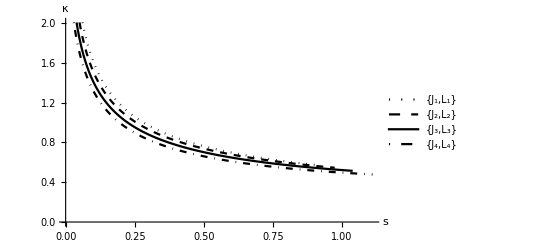

```mathematica
ListLinePlot[{CSCurvatureofLoC[200,923,1],CSCurvatureofLoC[400,975,1],CSCurvatureofLoC[600,1040,1],CSCurvatureofLoC[800,1112,1]},AxesLabel->{"s","κ"},PlotStyle->{{Dotted,Black},{Dashed,Black},{Black},{DotDashed,Black}},PlotLegends->LineLegend[{{{"J_1,L_1"},{"J_2,L_2"},{"J_3,L_3"},{"J_4,L_4"}}},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5]]
```

### Torsion

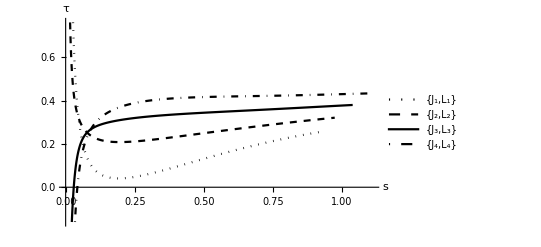

```mathematica
ListLinePlot[{CSTorsionofLoC[200,923,1],CSTorsionofLoC[400,975,1],CSTorsionofLoC[600,1040,1],CSTorsionofLoC[800,1112,1]},AxesLabel->{"s","τ"},PlotStyle->{{Dotted,Black},{Dashed,Black},{Black},{DotDashed,Black}},PlotLegends->LineLegend[{{{"J_1,L_1"},{"J_2,L_2"},{"J_3,L_3"},{"J_4,L_4"}}},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5]]
```

### Derivative of Curvature

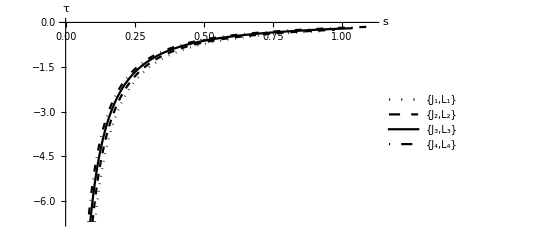

```mathematica
ListLinePlot[{CSDerivativeCurvatureofLoC[200,923,1],CSDerivativeCurvatureofLoC[400,975,1],CSDerivativeCurvatureofLoC[600,1040,1],CSDerivativeCurvatureofLoC[800,1112,1]},AxesLabel->{"s","τ"},PlotStyle->{{Dotted,Black},{Dashed,Black},{Black},{DotDashed,Black}},PlotLegends->LineLegend[{{{"J_1,L_1"},{"J_2,L_2"},{"J_3,L_3"},{"J_4,L_4"}}},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5]]
```

### LCG

#### Set up

```mathematica
CSCurvatureofLoC2[v_,nn_,optimum_]:=Module[{opt1=optimum,pu, pv,u1x1, u1x2, u1x3,u1t1, u1t2, u1t3,u1dt1, u1dt2, u1dt3,u1d2t1, u1d2t2, u1d2t3,u1d3t1, u1d3t2, u1d3t3,u2x1, u2x2, u2x3,u2t1, u2t2, u2t3,u2dt1, u2dt2, u2dt3,u2d2t1, u2d2t2, u2d2t3,u2d3t1, u2d3t2, u2d3t3,v1x1, v1x2, v1x3,v1t1, v1t2, v1t3,v1dt1, v1dt2, v1dt3,v1d2t1, v1d2t2, v1d2t3,v1d3t1, v1d3t2, v1d3t3,v2x1, v2x2, v2x3,v2t1, v2t2, v2t3,v2dt1, v2dt2, v2dt3,v2d2t1, v2d2t2, v2d2t3,v2d3t1, v2d3t2, v2d3t3, D2uDs2, D2vDs2, GeoCur,Cur},
pu=CUDAMemoryAllocate["Float",nn];
pv=CUDAMemoryAllocate["Float",nn];
u1x1=CUDAMemoryAllocate["Float",nn];
u1x2=CUDAMemoryAllocate["Float",nn];
u1x3=CUDAMemoryAllocate["Float",nn];
u1t1=CUDAMemoryAllocate["Float",nn];
u1t2=CUDAMemoryAllocate["Float",nn];
u1t3=CUDAMemoryAllocate["Float",nn];
u1dt1=CUDAMemoryAllocate["Float",nn];
u1dt2=CUDAMemoryAllocate["Float",nn];
u1dt3=CUDAMemoryAllocate["Float",nn];
u1d2t1=CUDAMemoryAllocate["Float",nn];
u1d2t2=CUDAMemoryAllocate["Float",nn];
u1d2t3=CUDAMemoryAllocate["Float",nn];
u1d3t1=CUDAMemoryAllocate["Float",nn];
u1d3t2=CUDAMemoryAllocate["Float",nn];
u1d3t3=CUDAMemoryAllocate["Float",nn];
u2x1=CUDAMemoryAllocate["Float",nn];
u2x2=CUDAMemoryAllocate["Float",nn];
u2x3=CUDAMemoryAllocate["Float",nn];
u2t1=CUDAMemoryAllocate["Float",nn];
u2t2=CUDAMemoryAllocate["Float",nn];
u2t3=CUDAMemoryAllocate["Float",nn];
u2dt1=CUDAMemoryAllocate["Float",nn];
u2dt2=CUDAMemoryAllocate["Float",nn];
u2dt3=CUDAMemoryAllocate["Float",nn];
u2d2t1=CUDAMemoryAllocate["Float",nn];
u2d2t2=CUDAMemoryAllocate["Float",nn];
u2d2t3=CUDAMemoryAllocate["Float",nn];
u2d3t1=CUDAMemoryAllocate["Float",nn];
u2d3t2=CUDAMemoryAllocate["Float",nn];
u2d3t3=CUDAMemoryAllocate["Float",nn];
v1x1=CUDAMemoryAllocate["Float",nn];
v1x2=CUDAMemoryAllocate["Float",nn];
v1x3=CUDAMemoryAllocate["Float",nn];
v1t1=CUDAMemoryAllocate["Float",nn];
v1t2=CUDAMemoryAllocate["Float",nn];
v1t3=CUDAMemoryAllocate["Float",nn];
v1dt1=CUDAMemoryAllocate["Float",nn];
v1dt2=CUDAMemoryAllocate["Float",nn];
v1dt3=CUDAMemoryAllocate["Float",nn];
v1d2t1=CUDAMemoryAllocate["Float",nn];
v1d2t2=CUDAMemoryAllocate["Float",nn];
v1d2t3=CUDAMemoryAllocate["Float",nn];
v1d3t1=CUDAMemoryAllocate["Float",nn];
v1d3t2=CUDAMemoryAllocate["Float",nn];
v1d3t3=CUDAMemoryAllocate["Float",nn];
v2x1=CUDAMemoryAllocate["Float",nn];
v2x2=CUDAMemoryAllocate["Float",nn];
v2x3=CUDAMemoryAllocate["Float",nn];
v2t1=CUDAMemoryAllocate["Float",nn];
v2t2=CUDAMemoryAllocate["Float",nn];
v2t3=CUDAMemoryAllocate["Float",nn];
v2dt1=CUDAMemoryAllocate["Float",nn];
v2dt2=CUDAMemoryAllocate["Float",nn];
v2dt3=CUDAMemoryAllocate["Float",nn];
v2d2t1=CUDAMemoryAllocate["Float",nn];
v2d2t2=CUDAMemoryAllocate["Float",nn];
v2d2t3=CUDAMemoryAllocate["Float",nn];
v2d3t1=CUDAMemoryAllocate["Float",nn];
v2d3t2=CUDAMemoryAllocate["Float",nn];
v2d3t3=CUDAMemoryAllocate["Float",nn];
D2uDs2=CUDAMemoryAllocate["Float",nn];
D2vDs2=CUDAMemoryAllocate["Float",nn];
GeoCur=CUDAMemoryAllocate["Float",nn];
Cur=CUDAMemoryAllocate["Float",nn];

CSAllDetails[pu, pv,u1x1, u1x2, u1x3,u1t1, u1t2, u1t3,u1dt1, u1dt2, u1dt3,u1d2t1, u1d2t2, u1d2t3,u1d3t1, u1d3t2, u1d3t3,u2x1, u2x2, u2x3,u2t1, u2t2, u2t3,u2dt1, u2dt2, u2dt3,u2d2t1, u2d2t2, u2d2t3,u2d3t1, u2d3t2, u2d3t3,v1x1, v1x2, v1x3,v1t1, v1t2, v1t3,v1dt1, v1dt2, v1dt3,v1d2t1, v1d2t2, v1d2t3,v1d3t1, v1d3t2, v1d3t3,v2x1, v2x2, v2x3,v2t1, v2t2, v2t3,v2dt1, v2dt2, v2dt3,v2d2t1, v2d2t2, v2d2t3,v2d3t1, v2d3t2, v2d3t3, D2uDs2, D2vDs2, GeoCur,v,optimum,nn];
CSCurvature[Cur,pu, pv,u1x1, u1x2, u1x3,u1t1, u1t2, u1t3,u1dt1, u1dt2, u1dt3,u1d2t1, u1d2t2, u1d2t3,u1d3t1, u1d3t2, u1d3t3,u2x1, u2x2, u2x3,u2t1, u2t2, u2t3,u2dt1, u2dt2, u2dt3,u2d2t1, u2d2t2, u2d2t3,u2d3t1, u2d3t2, u2d3t3,v1x1, v1x2, v1x3,v1t1, v1t2, v1t3,v1dt1, v1dt2, v1dt3,v1d2t1, v1d2t2, v1d2t3,v1d3t1, v1d3t2, v1d3t3,v2x1, v2x2, v2x3,v2t1, v2t2, v2t3,v2dt1, v2dt2, v2dt3,v2d2t1, v2d2t2, v2d2t3,v2d3t1, v2d3t2, v2d3t3, D2uDs2, D2vDs2, GeoCur,optimum,nn];
CUDAMemoryGet[Cur]];
```

#### Four

```mathematica
1/CSCurvatureofLoC2[200,923,1]
```

{0.161162,0.173712,0.185167,0.195768,0.20568,0.215022,0.223882,0.232329,0.240417,0.248188,0.255678,0.262917,0.269928,0.276732,0.283347,0.289789,0.29607,0.302203,0.308197,0.314063,0.319807,0.325439,0.330963,0.336387,0.341715,0.346953,0.352105,0.357175,0.362168,0.367086,0.371934,0.376713,0.381428,0.386079,0.390671,0.395205,0.399684,0.404109,0.408482,0.412805,0.41708,0.421309,0.425492,0.429632,0.433729,0.437786,0.441802,0.44578,0.44972,0.453624,0.457492,0.461325,0.465125,0.468892,0.472627,0.476331,0.480005,0.483648,0.487263,0.490849,0.494408,0.49794,0.501446,0.504925,0.508379,0.511809,0.515214,0.518595,0.521954,0.525289,0.528602,0.531894,0.535163,0.538412,0.54164,0.544848,0.548036,0.551204,0.554353,0.557483,0.560595,0.563689,0.566765,0.569822,0.572863,0.575887,0.578894,0.581884,0.584858,0.587817,0.590759,0.593686,0.596598,0.599495,0.602377,0.605245,0.608098,0.610937,0.613762,0.616573,0.619371,0.622155,0.624927,0.627685,0.630431,0.633163,0.635884,0.638592,0.641288,0.643971,0.646643,0.649304,0.651953,0.65459,0.657216,0.659831,0.662436,0.665029,0.667611,0.670183,0.672745,0.675296,0.677837,0.680368,0.682888,0.6854,0.687901,0.690392,0.692874,0.695347,0.69781,0.700264,0.702709,0.705145,0.707572,0.70999,0.712399,0.7148,0.717192,0.719575,0.721951,0.724317,0.726676,0.729026,0.731369,0.733704,0.73603,0.738349,0.74066,0.742963,0.745259,0.747547,0.749828,0.752101,0.754367,0.756625,0.758877,0.761121,0.763359,0.765589,0.767812,0.770029,0.772239,0.774442,0.776638,0.778828,0.781011,0.783187,0.785357,0.787521,0.789678,0.791829,0.793974,0.796113,0.798245,0.800371,0.802492,0.804606,0.806714,0.808817,0.810914,0.813005,0.81509,0.817169,0.819243,0.821311,0.823374,0.825431,0.827482,0.829528,0.831569,0.833604,0.835634,0.837659,0.839678,0.841692,0.843701,0.845705,0.847704,0.849698,0.851687,0.85367,0.855649,0.857623,0.859592,0.861556,0.863516,0.865471,0.86742,0.869366,0.871306,0.873242,0.875173,0.8771,0.879022,0.88094,0.882853,0.884761,0.886666,0.888566,0.890461,0.892352,0.894239,0.896122,0.898,0.899874,0.901744,0.90361,0.905472,0.907329,0.909183,0.911032,0.912877,0.914719,0.916556,0.918389,0.920219,0.922044,0.923866,0.925684,0.927498,0.929308,0.931114,0.932917,0.934715,0.93651,0.938302,0.940089,0.941873,0.943654,0.94543,0.947203,0.948973,0.950739,0.952502,0.95426,0.956016,0.957768,0.959516,0.961262,0.963003,0.964741,0.966476,0.968208,0.969936,0.971661,0.973383,0.975102,0.976817,0.978529,0.980237,0.981943,0.983645,0.985344,0.98704,0.988733,0.990423,0.992109,0.993793,0.995473,0.997151,0.998825,1.0005,1.00216,1.00383,1.00549,1.00715,1.00881,1.01046,1.01211,1.01376,1.0154,1.01705,1.01869,1.02032,1.02196,1.02359,1.02521,1.02684,1.02846,1.03008,1.0317,1.03331,1.03492,1.03653,1.03814,1.03974,1.04134,1.04294,1.04453,1.04613,1.04772,1.0493,1.05089,1.05247,1.05405,1.05563,1.0572,1.05878,1.06034,1.06191,1.06348,1.06504,1.0666,1.06816,1.06971,1.07126,1.07281,1.07436,1.07591,1.07745,1.07899,1.08053,1.08206,1.0836,1.08513,1.08665,1.08818,1.08971,1.09123,1.09275,1.09426,1.09578,1.09729,1.0988,1.10031,1.10182,1.10332,1.10482,1.10632,1.10782,1.10931,1.11081,1.1123,1.11379,1.11527,1.11676,1.11824,1.11972,1.1212,1.12267,1.12415,1.12562,1.12709,1.12856,1.13002,1.13148,1.13295,1.13441,1.13586,1.13732,1.13877,1.14022,1.14167,1.14312,1.14457,1.14601,1.14745,1.14889,1.15033,1.15176,1.1532,1.15463,1.15606,1.15749,1.15892,1.16034,1.16176,1.16318,1.1646,1.16602,1.16744,1.16885,1.17026,1.17167,1.17308,1.17448,1.17589,1.17729,1.17869,1.18009,1.18149,1.18288,1.18428,1.18567,1.18706,1.18845,1.18983,1.19122,1.1926,1.19398,1.19536,1.19674,1.19812,1.19949,1.20087,1.20224,1.20361,1.20498,1.20634,1.20771,1.20907,1.21043,1.21179,1.21315,1.21451,1.21586,1.21722,1.21857,1.21992,1.22127,1.22262,1.22396,1.22531,1.22665,1.22799,1.22933,1.23067,1.232,1.23334,1.23467,1.236,1.23733,1.23866,1.23999,1.24131,1.24264,1.24396,1.24528,1.2466,1.24792,1.24923,1.25055,1.25186,1.25317,1.25449,1.2558,1.2571,1.25841,1.25971,1.26102,1.26232,1.26362,1.26492,1.26622,1.26751,1.26881,1.2701,1.2714,1.27269,1.27398,1.27526,1.27655,1.27784,1.27912,1.2804,1.28168,1.28296,1.28424,1.28552,1.2868,1.28807,1.28934,1.29062,1.29189,1.29316,1.29442,1.29569,1.29695,1.29822,1.29948,1.30074,1.302,1.30326,1.30452,1.30578,1.30703,1.30828,1.30954,1.31079,1.31204,1.31329,1.31453,1.31578,1.31703,1.31827,1.31951,1.32075,1.32199,1.32323,1.32447,1.32571,1.32694,1.32818,1.32941,1.33064,1.33187,1.3331,1.33433,1.33555,1.33678,1.338,1.33923,1.34045,1.34167,1.34289,1.34411,1.34533,1.34654,1.34776,1.34897,1.35018,1.3514,1.35261,1.35382,1.35502,1.35623,1.35744,1.35864,1.35985,1.36105,1.36225,1.36345,1.36465,1.36585,1.36704,1.36824,1.36944,1.37063,1.37182,1.37301,1.3742,1.37539,1.37658,1.37777,1.37896,1.38014,1.38132,1.38251,1.38369,1.38487,1.38605,1.38723,1.38841,1.38958,1.39076,1.39193,1.39311,1.39428,1.39545,1.39662,1.39779,1.39896,1.40013,1.4013,1.40246,1.40362,1.40479,1.40595,1.40711,1.40827,1.40943,1.41059,1.41175,1.4129,1.41406,1.41521,1.41637,1.41752,1.41867,1.41982,1.42097,1.42212,1.42327,1.42441,1.42556,1.4267,1.42785,1.42899,1.43013,1.43127,1.43241,1.43355,1.43469,1.43583,1.43696,1.4381,1.43923,1.44037,1.4415,1.44263,1.44376,1.44489,1.44602,1.44715,1.44827,1.4494,1.45053,1.45165,1.45277,1.4539,1.45502,1.45614,1.45726,1.45838,1.45949,1.46061,1.46173,1.46284,1.46396,1.46507,1.46618,1.46729,1.4684,1.46951,1.47062,1.47173,1.47284,1.47394,1.47505,1.47615,1.47726,1.47836,1.47946,1.48056,1.48166,1.48276,1.48386,1.48496,1.48606,1.48715,1.48825,1.48934,1.49044,1.49153,1.49262,1.49371,1.4948,1.49589,1.49698,1.49807,1.49915,1.50024,1.50132,1.50241,1.50349,1.50457,1.50566,1.50674,1.50782,1.5089,1.50998,1.51105,1.51213,1.51321,1.51428,1.51536,1.51643,1.5175,1.51858,1.51965,1.52072,1.52179,1.52286,1.52393,1.52499,1.52606,1.52713,1.52819,1.52926,1.53032,1.53138,1.53244,1.53351,1.53457,1.53563,1.53668,1.53774,1.5388,1.53986,1.54091,1.54197,1.54302,1.54408,1.54513,1.54618,1.54723,1.54828,1.54933,1.55038,1.55143,1.55248,1.55352,1.55457,1.55561,1.55666,1.5577,1.55875,1.55979,1.56083,1.56187,1.56291,1.56395,1.56499,1.56603,1.56706,1.5681,1.56914,1.57017,1.5712,1.57224,1.57327,1.5743,1.57533,1.57637,1.5774,1.57842,1.57945,1.58048,1.58151,1.58253,1.58356,1.58458,1.58561,1.58663,1.58766,1.58868,1.5897,1.59072,1.59174,1.59276,1.59378,1.5948,1.59581,1.59683,1.59784,1.59886,1.59987,1.60089,1.6019,1.60291,1.60393,1.60494,1.60595,1.60696,1.60796,1.60897,1.60998,1.61099,1.61199,1.613,1.614,1.61501,1.61601,1.61701,1.61802,1.61902,1.62002,1.62102,1.62202,1.62302,1.62401,1.62501,1.62601,1.627,1.628,1.62899,1.62999,1.63098,1.63198,1.63297,1.63396,1.63495,1.63594,1.63693,1.63792,1.63891,1.63989,1.64088,1.64187,1.64285,1.64384,1.64482,1.64581,1.64679,1.64777,1.64875,1.64973,1.65071,1.65169,1.65267,1.65365,1.65463,1.65561,1.65658,1.65756,1.65853,1.65951,1.66048,1.66146,1.66243,1.6634,1.66437,1.66534,1.66631,1.66728,1.66825,1.66922,1.67019,1.67115,1.67212,1.67309,1.67405,1.67502,1.67598,1.67694,1.67791,1.67887,1.67983,1.68079,1.68175,1.68271,1.68367,1.68463,1.68558,1.68654,1.6875,1.68845,1.68941,1.69036,1.69132,1.69227,1.69322,1.69418,1.69513,1.69608,1.69703,1.69798,1.69893,1.69988,1.70082,1.70177,1.70272,1.70366,1.70461,1.70555,1.7065,1.70744,1.70839,1.70933,1.71027,1.71121,1.71215,1.71309,1.71403,1.71497,1.71591,1.71685,1.71778,1.71872,1.71966,1.72059,1.72152,1.72246,1.72339,1.72433,1.72526,1.72619,1.72712,1.72805,1.72898,1.72991,1.73084,1.73177,1.73269,1.73362,1.73455,1.73547,1.7364,1.73732,1.73825,1.73917,1.74009,1.74102,1.74194,1.74286,1.74378,1.7447,1.74562,1.74654,1.74746,1.74837,1.74929,1.75021,1.75112,1.75204,1.75295,1.75387,1.75478,1.75569,1.75661,1.75752,1.75795}

```mathematica
1/CSCurvatureofLoC2[400,975,1]
```

{0.203244,0.215609,0.226886,0.237316,0.247067,0.256258,0.264978,0.273294,0.281261,0.28892,0.296307,0.30345,0.310374,0.317097,0.323639,0.330014,0.336234,0.342311,0.348256,0.354076,0.359781,0.365376,0.370869,0.376265,0.381569,0.386787,0.391921,0.396978,0.401959,0.406869,0.41171,0.416486,0.421199,0.425852,0.430447,0.434986,0.439471,0.443904,0.448287,0.452622,0.45691,0.461153,0.465352,0.469509,0.473624,0.4777,0.481736,0.485735,0.489697,0.493624,0.497516,0.501373,0.505198,0.508991,0.512752,0.516483,0.520184,0.523856,0.527499,0.531115,0.534703,0.538264,0.5418,0.54531,0.548795,0.552255,0.555692,0.559105,0.562495,0.565862,0.569208,0.572531,0.575834,0.579115,0.582376,0.585617,0.588838,0.592039,0.595221,0.598385,0.60153,0.604657,0.607766,0.610857,0.613931,0.616988,0.620028,0.623052,0.626059,0.629051,0.632027,0.634987,0.637932,0.640862,0.643777,0.646677,0.649563,0.652435,0.655292,0.658136,0.660966,0.663783,0.666586,0.669377,0.672154,0.674919,0.677671,0.68041,0.683137,0.685853,0.688556,0.691247,0.693927,0.696595,0.699251,0.701897,0.704531,0.707154,0.709767,0.712368,0.714959,0.71754,0.72011,0.72267,0.725219,0.727759,0.730289,0.732809,0.735319,0.737819,0.74031,0.742792,0.745264,0.747727,0.750181,0.752626,0.755062,0.757489,0.759907,0.762317,0.764718,0.76711,0.769494,0.77187,0.774238,0.776597,0.778948,0.781292,0.783627,0.785954,0.788274,0.790586,0.79289,0.795187,0.797476,0.799758,0.802032,0.804299,0.806559,0.808811,0.811057,0.813295,0.815526,0.817751,0.819968,0.822179,0.824383,0.82658,0.828771,0.830955,0.833133,0.835304,0.837468,0.839626,0.841778,0.843924,0.846063,0.848196,0.850324,0.852445,0.854559,0.856668,0.858771,0.860868,0.86296,0.865045,0.867125,0.869199,0.871267,0.87333,0.875387,0.877438,0.879484,0.881525,0.88356,0.88559,0.887614,0.889633,0.891647,0.893656,0.895659,0.897657,0.89965,0.901638,0.903621,0.905599,0.907572,0.909541,0.911504,0.913462,0.915415,0.917364,0.919308,0.921247,0.923181,0.925111,0.927036,0.928957,0.930873,0.932784,0.934691,0.936593,0.938491,0.940384,0.942273,0.944158,0.946038,0.947914,0.949785,0.951653,0.953516,0.955375,0.95723,0.95908,0.960927,0.962769,0.964607,0.966441,0.968271,0.970097,0.971919,0.973737,0.975552,0.977362,0.979168,0.980971,0.982769,0.984564,0.986355,0.988142,0.989926,0.991705,0.993481,0.995253,0.997022,0.998787,1.00055,1.00231,1.00406,1.00581,1.00756,1.0093,1.01104,1.01278,1.01451,1.01624,1.01797,1.01969,1.02141,1.02312,1.02484,1.02655,1.02825,1.02995,1.03165,1.03335,1.03504,1.03673,1.03842,1.0401,1.04178,1.04346,1.04513,1.0468,1.04847,1.05013,1.0518,1.05345,1.05511,1.05676,1.05841,1.06006,1.0617,1.06334,1.06498,1.06661,1.06824,1.06987,1.07149,1.07312,1.07474,1.07635,1.07797,1.07958,1.08119,1.08279,1.0844,1.086,1.08759,1.08919,1.09078,1.09237,1.09395,1.09554,1.09712,1.0987,1.10027,1.10184,1.10342,1.10498,1.10655,1.10811,1.10967,1.11123,1.11278,1.11433,1.11588,1.11743,1.11898,1.12052,1.12206,1.12359,1.12513,1.12666,1.12819,1.12972,1.13124,1.13277,1.13429,1.1358,1.13732,1.13883,1.14034,1.14185,1.14336,1.14486,1.14636,1.14786,1.14936,1.15085,1.15234,1.15383,1.15532,1.15681,1.15829,1.15977,1.16125,1.16272,1.1642,1.16567,1.16714,1.16861,1.17007,1.17154,1.173,1.17446,1.17591,1.17737,1.17882,1.18027,1.18172,1.18317,1.18461,1.18605,1.18749,1.18893,1.19037,1.1918,1.19323,1.19466,1.19609,1.19752,1.19894,1.20036,1.20178,1.2032,1.20462,1.20603,1.20744,1.20885,1.21026,1.21167,1.21307,1.21448,1.21588,1.21728,1.21867,1.22007,1.22146,1.22285,1.22424,1.22563,1.22702,1.2284,1.22978,1.23116,1.23254,1.23392,1.23529,1.23666,1.23804,1.23941,1.24077,1.24214,1.2435,1.24486,1.24623,1.24758,1.24894,1.2503,1.25165,1.253,1.25435,1.2557,1.25705,1.25839,1.25974,1.26108,1.26242,1.26376,1.26509,1.26643,1.26776,1.26909,1.27042,1.27175,1.27308,1.2744,1.27573,1.27705,1.27837,1.27969,1.28101,1.28232,1.28364,1.28495,1.28626,1.28757,1.28888,1.29018,1.29149,1.29279,1.29409,1.29539,1.29669,1.29799,1.29928,1.30058,1.30187,1.30316,1.30445,1.30574,1.30702,1.30831,1.30959,1.31087,1.31216,1.31343,1.31471,1.31599,1.31726,1.31854,1.31981,1.32108,1.32235,1.32361,1.32488,1.32615,1.32741,1.32867,1.32993,1.33119,1.33245,1.3337,1.33496,1.33621,1.33746,1.33871,1.33996,1.34121,1.34246,1.3437,1.34495,1.34619,1.34743,1.34867,1.34991,1.35115,1.35238,1.35362,1.35485,1.35608,1.35731,1.35854,1.35977,1.361,1.36222,1.36345,1.36467,1.36589,1.36711,1.36833,1.36955,1.37076,1.37198,1.37319,1.3744,1.37561,1.37682,1.37803,1.37924,1.38045,1.38165,1.38286,1.38406,1.38526,1.38646,1.38766,1.38886,1.39005,1.39125,1.39244,1.39364,1.39483,1.39602,1.39721,1.39839,1.39958,1.40077,1.40195,1.40313,1.40432,1.4055,1.40668,1.40786,1.40903,1.41021,1.41139,1.41256,1.41373,1.4149,1.41607,1.41724,1.41841,1.41958,1.42074,1.42191,1.42307,1.42424,1.4254,1.42656,1.42772,1.42887,1.43003,1.43119,1.43234,1.4335,1.43465,1.4358,1.43695,1.4381,1.43925,1.4404,1.44154,1.44269,1.44383,1.44497,1.44612,1.44726,1.4484,1.44953,1.45067,1.45181,1.45294,1.45408,1.45521,1.45634,1.45748,1.45861,1.45973,1.46086,1.46199,1.46312,1.46424,1.46537,1.46649,1.46761,1.46873,1.46985,1.47097,1.47209,1.4732,1.47432,1.47544,1.47655,1.47766,1.47877,1.47988,1.48099,1.4821,1.48321,1.48432,1.48542,1.48653,1.48763,1.48874,1.48984,1.49094,1.49204,1.49314,1.49424,1.49533,1.49643,1.49752,1.49862,1.49971,1.5008,1.5019,1.50299,1.50408,1.50516,1.50625,1.50734,1.50842,1.50951,1.51059,1.51167,1.51276,1.51384,1.51492,1.516,1.51708,1.51815,1.51923,1.5203,1.52138,1.52245,1.52353,1.5246,1.52567,1.52674,1.52781,1.52888,1.52994,1.53101,1.53207,1.53314,1.5342,1.53527,1.53633,1.53739,1.53845,1.53951,1.54057,1.54162,1.54268,1.54374,1.54479,1.54584,1.5469,1.54795,1.549,1.55005,1.5511,1.55215,1.5532,1.55424,1.55529,1.55634,1.55738,1.55842,1.55947,1.56051,1.56155,1.56259,1.56363,1.56467,1.5657,1.56674,1.56778,1.56881,1.56984,1.57088,1.57191,1.57294,1.57397,1.575,1.57603,1.57706,1.57809,1.57911,1.58014,1.58116,1.58219,1.58321,1.58423,1.58526,1.58628,1.5873,1.58832,1.58933,1.59035,1.59137,1.59238,1.5934,1.59441,1.59543,1.59644,1.59745,1.59846,1.59947,1.60048,1.60149,1.6025,1.60351,1.60451,1.60552,1.60652,1.60753,1.60853,1.60953,1.61053,1.61153,1.61253,1.61353,1.61453,1.61553,1.61653,1.61752,1.61852,1.61951,1.62051,1.6215,1.62249,1.62348,1.62447,1.62546,1.62645,1.62744,1.62843,1.62941,1.6304,1.63139,1.63237,1.63335,1.63434,1.63532,1.6363,1.63728,1.63826,1.63924,1.64022,1.64119,1.64217,1.64315,1.64412,1.6451,1.64607,1.64704,1.64802,1.64899,1.64996,1.65093,1.6519,1.65287,1.65383,1.6548,1.65577,1.65673,1.6577,1.65866,1.65962,1.66059,1.66155,1.66251,1.66347,1.66443,1.66539,1.66635,1.6673,1.66826,1.66922,1.67017,1.67113,1.67208,1.67303,1.67399,1.67494,1.67589,1.67684,1.67779,1.67874,1.67968,1.68063,1.68158,1.68252,1.68347,1.68441,1.68536,1.6863,1.68724,1.68818,1.68912,1.69006,1.691,1.69194,1.69288,1.69382,1.69475,1.69569,1.69662,1.69756,1.69849,1.69942,1.70036,1.70129,1.70222,1.70315,1.70408,1.70501,1.70593,1.70686,1.70779,1.70871,1.70964,1.71056,1.71149,1.71241,1.71333,1.71425,1.71517,1.71609,1.71701,1.71793,1.71885,1.71977,1.72068,1.7216,1.72251,1.72343,1.72434,1.72526,1.72617,1.72708,1.72799,1.7289,1.72981,1.73072,1.73163,1.73254,1.73344,1.73435,1.73526,1.73616,1.73706,1.73797,1.73887,1.73977,1.74067,1.74158,1.74248,1.74337,1.74427,1.74517,1.74607,1.74697,1.74786,1.74876,1.74965,1.75054,1.75144,1.75233,1.75322,1.75411,1.755,1.75589,1.75678,1.75767,1.75856,1.75945,1.76033,1.76122,1.7621,1.76299,1.76387,1.76476,1.76564,1.76652,1.7674,1.76828,1.76916,1.77004,1.77092,1.7718,1.77267,1.77355,1.77442,1.7753,1.77617,1.77705,1.77792,1.77879,1.77966,1.78053,1.7814,1.78227,1.78314,1.78401,1.78488,1.78575,1.78661,1.78748,1.78834,1.78921,1.79007,1.79093,1.7918,1.79266,1.79352,1.79438,1.79524,1.7961,1.79695,1.79781,1.79867,1.79953,1.80038,1.80124,1.80209,1.80294,1.8038,1.80465,1.8055,1.80635,1.8072,1.80805,1.8089,1.80975,1.8106,1.81144,1.81229,1.81314,1.81398,1.81482,1.81567,1.81651,1.81735,1.81819,1.81904,1.81988,1.82072,1.82156,1.82239,1.82323,1.82407,1.8249,1.82574,1.82657,1.82741,1.82824,1.82908,1.82991,1.83074,1.83157,1.83237}

```mathematica
1/CSCurvatureofLoC2[600,1040,1]
```

{0.252865,0.264552,0.27525,0.285174,0.294476,0.303264,0.311621,0.319609,0.327278,0.334667,0.341808,0.348727,0.355447,0.361986,0.368359,0.37458,0.380662,0.386614,0.392445,0.398163,0.403776,0.40929,0.414711,0.420043,0.425291,0.43046,0.435554,0.440575,0.445528,0.450415,0.455239,0.460003,0.464709,0.469359,0.473955,0.4785,0.482995,0.487441,0.491842,0.496197,0.500508,0.504777,0.509005,0.513193,0.517343,0.521455,0.52553,0.52957,0.533576,0.537547,0.541486,0.545393,0.549268,0.553113,0.556928,0.560714,0.564472,0.568202,0.571904,0.57558,0.57923,0.582854,0.586454,0.590028,0.593579,0.597107,0.600611,0.604093,0.607552,0.61099,0.614406,0.617801,0.621176,0.62453,0.627864,0.631179,0.634474,0.637751,0.641009,0.644249,0.64747,0.650674,0.65386,0.657029,0.660181,0.663317,0.666436,0.669539,0.672626,0.675697,0.678753,0.681793,0.684819,0.687829,0.690825,0.693807,0.696774,0.699727,0.702667,0.705592,0.708505,0.711403,0.714289,0.717162,0.720021,0.722868,0.725703,0.728525,0.731335,0.734133,0.736919,0.739693,0.742456,0.745207,0.747946,0.750675,0.753392,0.756098,0.758794,0.761478,0.764152,0.766816,0.769469,0.772111,0.774744,0.777366,0.779979,0.782581,0.785174,0.787757,0.79033,0.792894,0.795449,0.797994,0.80053,0.803057,0.805575,0.808084,0.810584,0.813076,0.815559,0.818033,0.820498,0.822956,0.825404,0.827845,0.830277,0.832701,0.835117,0.837525,0.839925,0.842318,0.844703,0.847079,0.849448,0.85181,0.854164,0.856511,0.85885,0.861182,0.863507,0.865824,0.868134,0.870437,0.872734,0.875023,0.877305,0.879581,0.881849,0.884111,0.886366,0.888615,0.890856,0.893092,0.895321,0.897543,0.899759,0.901969,0.904172,0.906369,0.90856,0.910745,0.912924,0.915097,0.917263,0.919424,0.921579,0.923727,0.92587,0.928007,0.930139,0.932265,0.934385,0.936499,0.938608,0.940711,0.942809,0.944901,0.946988,0.949069,0.951145,0.953216,0.955281,0.957341,0.959396,0.961446,0.96349,0.965529,0.967564,0.969593,0.971617,0.973636,0.975651,0.97766,0.979664,0.981664,0.983659,0.985649,0.987634,0.989614,0.99159,0.993561,0.995527,0.997489,0.999446,1.0014,1.00335,1.00529,1.00723,1.00916,1.01109,1.01302,1.01494,1.01686,1.01877,1.02068,1.02258,1.02448,1.02638,1.02827,1.03016,1.03204,1.03392,1.03579,1.03766,1.03953,1.04139,1.04325,1.04511,1.04696,1.0488,1.05065,1.05248,1.05432,1.05615,1.05798,1.0598,1.06162,1.06344,1.06525,1.06706,1.06886,1.07066,1.07246,1.07425,1.07604,1.07783,1.07961,1.08139,1.08317,1.08494,1.08671,1.08847,1.09023,1.09199,1.09375,1.0955,1.09725,1.09899,1.10073,1.10247,1.1042,1.10593,1.10766,1.10939,1.11111,1.11282,1.11454,1.11625,1.11796,1.11966,1.12136,1.12306,1.12476,1.12645,1.12814,1.12982,1.13151,1.13319,1.13486,1.13654,1.13821,1.13987,1.14154,1.1432,1.14486,1.14651,1.14817,1.14981,1.15146,1.1531,1.15475,1.15638,1.15802,1.15965,1.16128,1.16291,1.16453,1.16615,1.16777,1.16938,1.171,1.17261,1.17421,1.17582,1.17742,1.17902,1.18061,1.18221,1.1838,1.18538,1.18697,1.18855,1.19013,1.19171,1.19328,1.19486,1.19643,1.19799,1.19956,1.20112,1.20268,1.20424,1.20579,1.20734,1.20889,1.21044,1.21198,1.21352,1.21506,1.2166,1.21813,1.21967,1.22119,1.22272,1.22425,1.22577,1.22729,1.22881,1.23032,1.23183,1.23334,1.23485,1.23636,1.23786,1.23936,1.24086,1.24236,1.24385,1.24534,1.24683,1.24832,1.24981,1.25129,1.25277,1.25425,1.25572,1.2572,1.25867,1.26014,1.26161,1.26307,1.26454,1.266,1.26746,1.26891,1.27037,1.27182,1.27327,1.27472,1.27616,1.27761,1.27905,1.28049,1.28193,1.28336,1.2848,1.28623,1.28766,1.28908,1.29051,1.29193,1.29335,1.29477,1.29619,1.29761,1.29902,1.30043,1.30184,1.30325,1.30465,1.30606,1.30746,1.30886,1.31026,1.31165,1.31305,1.31444,1.31583,1.31722,1.3186,1.31999,1.32137,1.32275,1.32413,1.32551,1.32688,1.32825,1.32963,1.331,1.33236,1.33373,1.33509,1.33646,1.33782,1.33917,1.34053,1.34189,1.34324,1.34459,1.34594,1.34729,1.34864,1.34998,1.35132,1.35266,1.354,1.35534,1.35668,1.35801,1.35934,1.36067,1.362,1.36333,1.36465,1.36598,1.3673,1.36862,1.36994,1.37126,1.37257,1.37389,1.3752,1.37651,1.37782,1.37913,1.38043,1.38173,1.38304,1.38434,1.38564,1.38693,1.38823,1.38952,1.39082,1.39211,1.3934,1.39469,1.39597,1.39726,1.39854,1.39982,1.4011,1.40238,1.40366,1.40493,1.40621,1.40748,1.40875,1.41002,1.41129,1.41255,1.41382,1.41508,1.41634,1.4176,1.41886,1.42012,1.42138,1.42263,1.42388,1.42514,1.42639,1.42763,1.42888,1.43013,1.43137,1.43261,1.43385,1.43509,1.43633,1.43757,1.4388,1.44004,1.44127,1.4425,1.44373,1.44496,1.44619,1.44741,1.44864,1.44986,1.45108,1.4523,1.45352,1.45474,1.45595,1.45717,1.45838,1.45959,1.4608,1.46201,1.46322,1.46442,1.46563,1.46683,1.46804,1.46924,1.47044,1.47163,1.47283,1.47403,1.47522,1.47641,1.4776,1.47879,1.47998,1.48117,1.48236,1.48354,1.48473,1.48591,1.48709,1.48827,1.48945,1.49063,1.4918,1.49298,1.49415,1.49532,1.49649,1.49766,1.49883,1.5,1.50116,1.50233,1.50349,1.50465,1.50581,1.50697,1.50813,1.50929,1.51045,1.5116,1.51275,1.51391,1.51506,1.51621,1.51736,1.5185,1.51965,1.52079,1.52194,1.52308,1.52422,1.52536,1.5265,1.52764,1.52877,1.52991,1.53104,1.53218,1.53331,1.53444,1.53557,1.5367,1.53782,1.53895,1.54007,1.5412,1.54232,1.54344,1.54456,1.54568,1.5468,1.54792,1.54903,1.55015,1.55126,1.55237,1.55348,1.55459,1.5557,1.55681,1.55791,1.55902,1.56012,1.56123,1.56233,1.56343,1.56453,1.56563,1.56673,1.56782,1.56892,1.57001,1.5711,1.5722,1.57329,1.57438,1.57547,1.57655,1.57764,1.57873,1.57981,1.58089,1.58198,1.58306,1.58414,1.58522,1.58629,1.58737,1.58845,1.58952,1.59059,1.59167,1.59274,1.59381,1.59488,1.59595,1.59701,1.59808,1.59915,1.60021,1.60127,1.60233,1.6034,1.60446,1.60551,1.60657,1.60763,1.60869,1.60974,1.61079,1.61185,1.6129,1.61395,1.615,1.61605,1.61709,1.61814,1.61919,1.62023,1.62128,1.62232,1.62336,1.6244,1.62544,1.62648,1.62752,1.62855,1.62959,1.63062,1.63166,1.63269,1.63372,1.63475,1.63578,1.63681,1.63784,1.63886,1.63989,1.64091,1.64194,1.64296,1.64398,1.645,1.64602,1.64704,1.64806,1.64907,1.65009,1.6511,1.65212,1.65313,1.65414,1.65515,1.65616,1.65717,1.65818,1.65919,1.66019,1.6612,1.6622,1.66321,1.66421,1.66521,1.66621,1.66721,1.66821,1.66921,1.6702,1.6712,1.67219,1.67319,1.67418,1.67517,1.67616,1.67715,1.67814,1.67913,1.68012,1.68111,1.68209,1.68307,1.68406,1.68504,1.68602,1.687,1.68798,1.68896,1.68994,1.69092,1.69189,1.69287,1.69384,1.69482,1.69579,1.69676,1.69773,1.6987,1.69967,1.70064,1.70161,1.70257,1.70354,1.7045,1.70546,1.70643,1.70739,1.70835,1.70931,1.71027,1.71123,1.71218,1.71314,1.7141,1.71505,1.716,1.71696,1.71791,1.71886,1.71981,1.72076,1.72171,1.72265,1.7236,1.72455,1.72549,1.72643,1.72738,1.72832,1.72926,1.7302,1.73114,1.73208,1.73302,1.73395,1.73489,1.73582,1.73676,1.73769,1.73862,1.73955,1.74049,1.74142,1.74234,1.74327,1.7442,1.74513,1.74605,1.74698,1.7479,1.74882,1.74974,1.75067,1.75159,1.75251,1.75342,1.75434,1.75526,1.75617,1.75709,1.758,1.75892,1.75983,1.76074,1.76165,1.76256,1.76347,1.76438,1.76529,1.76619,1.7671,1.768,1.76891,1.76981,1.77071,1.77161,1.77251,1.77341,1.77431,1.77521,1.77611,1.77701,1.7779,1.77879,1.77969,1.78058,1.78147,1.78237,1.78326,1.78415,1.78503,1.78592,1.78681,1.7877,1.78858,1.78947,1.79035,1.79123,1.79211,1.793,1.79388,1.79476,1.79563,1.79651,1.79739,1.79826,1.79914,1.80001,1.80089,1.80176,1.80263,1.8035,1.80438,1.80524,1.80611,1.80698,1.80785,1.80871,1.80958,1.81044,1.81131,1.81217,1.81303,1.81389,1.81476,1.81561,1.81647,1.81733,1.81819,1.81905,1.8199,1.82076,1.82161,1.82246,1.82331,1.82417,1.82502,1.82587,1.82672,1.82756,1.82841,1.82926,1.8301,1.83095,1.83179,1.83263,1.83348,1.83432,1.83516,1.836,1.83684,1.83768,1.83851,1.83935,1.84019,1.84102,1.84186,1.84269,1.84352,1.84435,1.84518,1.84602,1.84684,1.84767,1.8485,1.84933,1.85015,1.85098,1.8518,1.85263,1.85345,1.85427,1.85509,1.85591,1.85673,1.85755,1.85837,1.85919,1.86,1.86082,1.86163,1.86245,1.86326,1.86407,1.86488,1.86569,1.8665,1.86731,1.86812,1.86893,1.86974,1.87054,1.87135,1.87215,1.87295,1.87376,1.87456,1.87536,1.87616,1.87696,1.87776,1.87855,1.87935,1.88015,1.88094,1.88174,1.88253,1.88332,1.88412,1.88491,1.8857,1.88649,1.88728,1.88806,1.88885,1.88964,1.89042,1.89121,1.89199,1.89278,1.89356,1.89434,1.89512,1.8959,1.89668,1.89746,1.89824,1.89901,1.89979,1.90056,1.90134,1.90211,1.90288,1.90365,1.90443,1.9052,1.90597,1.90673,1.9075,1.90827,1.90904,1.9098,1.91057,1.91133,1.91209,1.91285,1.91362,1.91438,1.91514,1.91589,1.91665,1.91741,1.91817,1.91892,1.91968,1.92043,1.92119,1.92194,1.92269,1.92344,1.92419,1.92494,1.92569,1.92644,1.92718,1.92793,1.92867,1.92942,1.93016,1.9309,1.93165,1.93239,1.93313,1.93387,1.93461,1.93534,1.93608,1.93682,1.93755,1.93829,1.93902,1.93975,1.94049,1.94122,1.94195,1.94268,1.94302}

```mathematica
1/CSCurvatureofLoC2[800,1112,1]
```

{0.309418,0.319938,0.329588,0.338572,0.347028,0.355055,0.362724,0.370091,0.377196,0.384074,0.39075,0.397246,0.40358,0.409767,0.415819,0.421748,0.427562,0.43327,0.438879,0.444395,0.449823,0.455169,0.460437,0.465631,0.470754,0.475811,0.480804,0.485735,0.490608,0.495425,0.500187,0.504898,0.509558,0.51417,0.518736,0.523256,0.527733,0.532167,0.53656,0.540913,0.545228,0.549505,0.553746,0.557951,0.562122,0.566258,0.570363,0.574435,0.578475,0.582486,0.586466,0.590417,0.59434,0.598235,0.602103,0.605944,0.609759,0.613549,0.617313,0.621053,0.624769,0.628461,0.63213,0.635777,0.639401,0.643003,0.646584,0.650143,0.653682,0.657201,0.660699,0.664178,0.667637,0.671077,0.674499,0.677902,0.681287,0.684654,0.688003,0.691335,0.69465,0.697948,0.70123,0.704495,0.707744,0.710978,0.714195,0.717397,0.720584,0.723756,0.726913,0.730056,0.733184,0.736298,0.739397,0.742483,0.745556,0.748614,0.75166,0.754692,0.757711,0.760717,0.76371,0.766691,0.76966,0.772616,0.77556,0.778493,0.781413,0.784322,0.787218,0.790104,0.792978,0.795841,0.798693,0.801534,0.804364,0.807184,0.809992,0.81279,0.815578,0.818356,0.821123,0.823881,0.826628,0.829365,0.832093,0.834811,0.837519,0.840218,0.842907,0.845587,0.848258,0.85092,0.853573,0.856216,0.858851,0.861477,0.864094,0.866703,0.869303,0.871894,0.874477,0.877052,0.879619,0.882177,0.884727,0.887269,0.889803,0.892329,0.894848,0.897358,0.899861,0.902356,0.904844,0.907323,0.909796,0.912261,0.914719,0.917169,0.919612,0.922048,0.924477,0.926899,0.929313,0.931721,0.934122,0.936516,0.938903,0.941283,0.943657,0.946024,0.948385,0.950739,0.953086,0.955427,0.957762,0.96009,0.962412,0.964727,0.967036,0.96934,0.971637,0.973927,0.976212,0.978491,0.980764,0.983031,0.985292,0.987547,0.989797,0.99204,0.994278,0.996511,0.998737,1.00096,1.00317,1.00538,1.00759,1.00979,1.01198,1.01417,1.01635,1.01853,1.0207,1.02287,1.02503,1.02718,1.02933,1.03148,1.03362,1.03576,1.03789,1.04001,1.04213,1.04425,1.04636,1.04846,1.05057,1.05266,1.05475,1.05684,1.05892,1.061,1.06307,1.06514,1.0672,1.06926,1.07131,1.07336,1.07541,1.07745,1.07948,1.08151,1.08354,1.08556,1.08758,1.0896,1.09161,1.09361,1.09561,1.09761,1.0996,1.10159,1.10357,1.10555,1.10753,1.1095,1.11146,1.11343,1.11539,1.11734,1.11929,1.12124,1.12318,1.12512,1.12705,1.12899,1.13091,1.13284,1.13475,1.13667,1.13858,1.14049,1.14239,1.14429,1.14619,1.14808,1.14997,1.15186,1.15374,1.15562,1.15749,1.15936,1.16123,1.16309,1.16495,1.16681,1.16866,1.17051,1.17236,1.1742,1.17604,1.17787,1.1797,1.18153,1.18336,1.18518,1.187,1.18881,1.19062,1.19243,1.19424,1.19604,1.19784,1.19963,1.20142,1.20321,1.205,1.20678,1.20856,1.21033,1.2121,1.21387,1.21564,1.2174,1.21916,1.22092,1.22267,1.22442,1.22617,1.22791,1.22965,1.23139,1.23313,1.23486,1.23659,1.23832,1.24004,1.24176,1.24348,1.24519,1.2469,1.24861,1.25032,1.25202,1.25372,1.25541,1.25711,1.2588,1.26049,1.26217,1.26386,1.26554,1.26721,1.26889,1.27056,1.27223,1.27389,1.27556,1.27722,1.27888,1.28053,1.28218,1.28383,1.28548,1.28713,1.28877,1.29041,1.29204,1.29368,1.29531,1.29694,1.29856,1.30019,1.30181,1.30343,1.30504,1.30665,1.30827,1.30987,1.31148,1.31308,1.31468,1.31628,1.31788,1.31947,1.32106,1.32265,1.32423,1.32582,1.3274,1.32898,1.33055,1.33213,1.3337,1.33527,1.33683,1.3384,1.33996,1.34152,1.34308,1.34463,1.34618,1.34773,1.34928,1.35083,1.35237,1.35391,1.35545,1.35699,1.35852,1.36005,1.36158,1.36311,1.36463,1.36616,1.36768,1.36919,1.37071,1.37222,1.37374,1.37525,1.37675,1.37826,1.37976,1.38126,1.38276,1.38426,1.38575,1.38724,1.38873,1.39022,1.39171,1.39319,1.39467,1.39615,1.39763,1.3991,1.40058,1.40205,1.40352,1.40498,1.40645,1.40791,1.40937,1.41083,1.41229,1.41374,1.41519,1.41665,1.41809,1.41954,1.42099,1.42243,1.42387,1.42531,1.42674,1.42818,1.42961,1.43104,1.43247,1.4339,1.43532,1.43675,1.43817,1.43959,1.441,1.44242,1.44383,1.44524,1.44665,1.44806,1.44947,1.45087,1.45228,1.45368,1.45507,1.45647,1.45786,1.45926,1.46065,1.46204,1.46343,1.46481,1.4662,1.46758,1.46896,1.47034,1.47171,1.47309,1.47446,1.47583,1.4772,1.47857,1.47993,1.4813,1.48266,1.48402,1.48538,1.48674,1.48809,1.48945,1.4908,1.49215,1.49349,1.49484,1.49619,1.49753,1.49887,1.50021,1.50155,1.50289,1.50422,1.50555,1.50688,1.50821,1.50954,1.51087,1.51219,1.51352,1.51484,1.51616,1.51747,1.51879,1.5201,1.52142,1.52273,1.52404,1.52535,1.52665,1.52796,1.52926,1.53056,1.53186,1.53316,1.53446,1.53575,1.53704,1.53834,1.53963,1.54092,1.5422,1.54349,1.54477,1.54605,1.54734,1.54861,1.54989,1.55117,1.55244,1.55372,1.55499,1.55626,1.55753,1.55879,1.56006,1.56132,1.56258,1.56384,1.5651,1.56636,1.56762,1.56887,1.57013,1.57138,1.57263,1.57388,1.57512,1.57637,1.57761,1.57886,1.5801,1.58134,1.58258,1.58381,1.58505,1.58628,1.58751,1.58874,1.58997,1.5912,1.59243,1.59365,1.59488,1.5961,1.59732,1.59854,1.59976,1.60097,1.60219,1.6034,1.60461,1.60583,1.60703,1.60824,1.60945,1.61065,1.61186,1.61306,1.61426,1.61546,1.61666,1.61786,1.61905,1.62024,1.62144,1.62263,1.62382,1.62501,1.62619,1.62738,1.62856,1.62975,1.63093,1.63211,1.63329,1.63446,1.63564,1.63681,1.63799,1.63916,1.64033,1.6415,1.64267,1.64383,1.645,1.64616,1.64733,1.64849,1.64965,1.6508,1.65196,1.65312,1.65427,1.65543,1.65658,1.65773,1.65888,1.66003,1.66117,1.66232,1.66346,1.66461,1.66575,1.66689,1.66803,1.66916,1.6703,1.67144,1.67257,1.6737,1.67483,1.67596,1.67709,1.67822,1.67934,1.68047,1.68159,1.68272,1.68384,1.68496,1.68607,1.68719,1.68831,1.68942,1.69054,1.69165,1.69276,1.69387,1.69498,1.69608,1.69719,1.6983,1.6994,1.7005,1.7016,1.7027,1.7038,1.7049,1.70599,1.70709,1.70818,1.70927,1.71037,1.71146,1.71254,1.71363,1.71472,1.7158,1.71689,1.71797,1.71905,1.72013,1.72121,1.72229,1.72336,1.72444,1.72551,1.72659,1.72766,1.72873,1.7298,1.73087,1.73193,1.733,1.73406,1.73513,1.73619,1.73725,1.73831,1.73937,1.74043,1.74148,1.74254,1.74359,1.74465,1.7457,1.74675,1.7478,1.74885,1.74989,1.75094,1.75198,1.75303,1.75407,1.75511,1.75615,1.75719,1.75823,1.75926,1.7603,1.76133,1.76237,1.7634,1.76443,1.76546,1.76649,1.76751,1.76854,1.76957,1.77059,1.77161,1.77263,1.77366,1.77467,1.77569,1.77671,1.77773,1.77874,1.77975,1.78077,1.78178,1.78279,1.7838,1.78481,1.78581,1.78682,1.78782,1.78883,1.78983,1.79083,1.79183,1.79283,1.79383,1.79483,1.79582,1.79682,1.79781,1.7988,1.79979,1.80078,1.80177,1.80276,1.80375,1.80473,1.80572,1.8067,1.80768,1.80867,1.80965,1.81063,1.8116,1.81258,1.81356,1.81453,1.81551,1.81648,1.81745,1.81842,1.81939,1.82036,1.82133,1.82229,1.82326,1.82422,1.82518,1.82614,1.8271,1.82806,1.82902,1.82998,1.83094,1.83189,1.83285,1.8338,1.83475,1.8357,1.83665,1.8376,1.83855,1.8395,1.84044,1.84139,1.84233,1.84327,1.84421,1.84515,1.84609,1.84703,1.84797,1.8489,1.84984,1.85077,1.85171,1.85264,1.85357,1.8545,1.85543,1.85635,1.85728,1.8582,1.85913,1.86005,1.86097,1.8619,1.86282,1.86373,1.86465,1.86557,1.86649,1.8674,1.86831,1.86923,1.87014,1.87105,1.87196,1.87287,1.87377,1.87468,1.87559,1.87649,1.87739,1.8783,1.8792,1.8801,1.881,1.88189,1.88279,1.88369,1.88458,1.88547,1.88637,1.88726,1.88815,1.88904,1.88993,1.89082,1.8917,1.89259,1.89347,1.89436,1.89524,1.89612,1.897,1.89788,1.89876,1.89963,1.90051,1.90139,1.90226,1.90313,1.904,1.90488,1.90575,1.90661,1.90748,1.90835,1.90922,1.91008,1.91094,1.91181,1.91267,1.91353,1.91439,1.91525,1.9161,1.91696,1.91782,1.91867,1.91952,1.92038,1.92123,1.92208,1.92293,1.92378,1.92462,1.92547,1.92631,1.92716,1.928,1.92884,1.92969,1.93053,1.93136,1.9322,1.93304,1.93388,1.93471,1.93554,1.93638,1.93721,1.93804,1.93887,1.9397,1.94053,1.94135,1.94218,1.943,1.94383,1.94465,1.94547,1.94629,1.94711,1.94793,1.94875,1.94957,1.95038,1.9512,1.95201,1.95282,1.95363,1.95444,1.95525,1.95606,1.95687,1.95767,1.95848,1.95928,1.96009,1.96089,1.96169,1.96249,1.96329,1.96409,1.96489,1.96568,1.96648,1.96727,1.96807,1.96886,1.96965,1.97044,1.97123,1.97202,1.9728,1.97359,1.97437,1.97516,1.97594,1.97672,1.9775,1.97828,1.97906,1.97984,1.98062,1.98139,1.98217,1.98294,1.98371,1.98449,1.98526,1.98603,1.9868,1.98756,1.98833,1.9891,1.98986,1.99062,1.99139,1.99215,1.99291,1.99367,1.99443,1.99518,1.99594,1.9967,1.99745,1.9982,1.99896,1.99971,2.00046,2.00121,2.00196,2.0027,2.00345,2.00419,2.00494,2.00568,2.00642,2.00717,2.00791,2.00865,2.00938,2.01012,2.01086,2.01159,2.01233,2.01306,2.01379,2.01452,2.01525,2.01598,2.01671,2.01744,2.01816,2.01889,2.01961,2.02033,2.02106,2.02178,2.0225,2.02321,2.02393,2.02465,2.02537,2.02608,2.02679,2.02751,2.02822,2.02893,2.02964,2.03035,2.03105,2.03176,2.03247,2.03317,2.03387,2.03458,2.03528,2.03598,2.03668,2.03738,2.03807,2.03877,2.03947,2.04016,2.04085,2.04154,2.04224,2.04293,2.04361,2.0443,2.04499,2.04568,2.04636,2.04704,2.04773,2.04841,2.04909,2.04977,2.05045,2.05113,2.0518,2.05248,2.05315,2.05383,2.0545,2.05517,2.05584,2.05651,2.05718,2.05785,2.05851,2.05918,2.05984,2.06051,2.06117,2.06183,2.06249,2.06315,2.06381,2.06447,2.06512,2.06578,2.06643,2.06708,2.06774,2.06839,2.06904,2.06969,2.07033,2.07098,2.07163,2.07227,2.07291,2.07356,2.0742,2.07484,2.07548,2.07612,2.07675,2.07739,2.07803,2.07866,2.07929,2.07993,2.08056,2.08119,2.08182,2.08244,2.08307,2.0837,2.08432,2.08495,2.08557,2.08619,2.08681,2.08743,2.08805,2.08867,2.08887}

```mathematica
CS2rho200[s_]:={0.16116161978666116,0.1737116244827339,0.18516717962881307,0.19576831299898864,0.20568010597691314,0.21502167696139488,0.22388176654144287,0.2323288341394275,0.2404165358820607,0.2481879274851462,0.2556782642350017,0.2629166627750215,0.2699275811176882,0.2767317590148536,0.28334695921302,0.2897885208397703,0.2960697437241152,0.30220253220738263,0.30819701282187406,0.31406256610354405,0.3198072694685721,0.3254385167907198,0.33096302391480364,0.3363866591053325,0.3417149539642946,0.34695290881639895,0.35210491260724613,0.357175405461356,0.3621679838557664,0.36708644285410463,0.37193378604166455,0.37671322938214885,0.3814275870742705,0.3860793592393996,0.39067125291782984,0.39520530294286005,0.39968370672241377,0.4041085826769453,0.40848182090607243,0.4128051254200829,0.4170802777589119,0.4213088053084678,0.4254922174247636,0.4296319241116462,0.4337293282563587,0.4377856581834882,0.4418021567104241,0.4457799632709885,0.4497201300898646,0.45362374107986636,0.45749189575961713,0.4613253883475497,0.46512507841624523,0.468892196708043,0.4726272961581927,0.476331211765096,0.48000452274769284,0.48364830270084275,0.48726301524706706,0.49084949192450783,0.49440825189370924,0.49794012092633416,0.5014455265669157,0.5049249487196433,0.5083791637344665,0.5118087589585971,0.5152138919309706,0.5185954426504563,0.5219536601214182,0.5252891025377302,0.5286023199851387,0.5318935458115595,0.5351634580026656,0.5384120972455299,0.5416401182378989,0.5448479745309178,0.5480359027655645,0.5512041966281732,0.5543532442612771,0.5574834940224397,0.5605952678576381,0.5636889031017912,0.5667645595674146,0.5698224012415087,0.5728632207221049,0.5758867312627262,0.5788936245506533,0.5818841274375384,0.5848583424888032,0.5878167756270204,0.5907593150702779,0.5936862490842869,0.5965982001080598,0.5994950256524968,0.6023771203477046,0.6052446113468357,0.6080978731745338,0.6109367819482285,0.6137618135829956,0.6165732098218256,0.6193710118605973,0.6221553733032513,0.6249266576415958,0.6276849300913078,0.6304305119479267,0.6331631308689112,0.6358836296014364,0.638591680061047,0.6412875460098874,0.6439714158214642,0.6466434483917567,0.6493038717703866,0.6519527827032086,0.6545901917065813,0.6572163795470722,0.659831492446704,0.6624356406870889,0.6650288439714248,0.6676113993785647,0.67018324923761,0.6727446682754268,0.6752959498623464,0.6778368584005438,0.680367822945891,0.6828884609250937,0.6853995075580082,0.6879007697156662,0.6903922844295644,0.6928742127159634,0.6953468437578203,0.6978100766520587,0.7002640491979144,0.7027088518311577,0.7051448220289837,0.7075717169972252,0.7099899552335873,0.7123991870677497,0.7147997908927576,0.7171919166667664,0.7195753543574558,0.7219505780263742,0.7243174549667886,0.7266761066497479,0.7290264100832653,0.7313690099526283,0.7337036104732535,0.7360300427301683,0.7383488537014271,0.7406596938334042,0.7429629994398954,0.7452586929884663,0.7475468996429537,0.7498276853179489,0.7521007849595049,0.7543666778266713,0.756625381498531,0.7588769182349484,0.7611213150148788,0.7633586035736025,0.7655888903105996,0.7678124286349114,0.7700287041635265,0.7722386162207147,0.7744417301148017,0.7766379642524309,0.7788276003255092,0.7810107844856023,0.7831872308280783,0.7853573121455768,0.7875210431625634,0.7896784421078593,0.791829381253977,0.7939740337819605,0.7961127308066084,0.798245281815924,0.8003714950624914,0.8024917917487667,0.8046060646287412,0.8067144396515454,0.8088172040729884,0.8109138698465437,0.8130045717047037,0.8150896873753235,0.8171692068383182,0.8192430422614001,0.8213111868222202,0.8233735551150633,0.8254307121411781,0.8274820937291307,0.8295281110340008,0.8315687734258289,0.8336040097540898,0.835633999311658,0.8376585923882045,0.8396779746048855,0.8416920838315927,0.8437012830008324,0.8457048355224324,0.8477038773072942,0.8496976741971759,0.8516865176059313,0.8536702718765138,0.8556493242614694,0.8576232818234358,0.8595921864757666,0.8615564365864214,0.8635158172629088,0.8654706470616214,0.8674203549609839,0.8693658027806082,0.8713061498870334,0.8732419965645394,0.8751734075069371,0.8770999914575732,0.8790222728183427,0.8809396764934169,0.882852919554964,0.8847614265227146,0.8866658316461162,0.8885656520119395,0.8904611539000868,0.8923523246922842,0.8942390575053818,0.8961217235654172,0.8980000286893853,0.899874061090026,0.9017441055493016,0.903610063426933,0.905471640110393,0.90732922425621,0.9091827193669738,0.9110320284697508,0.9128773521510861,0.914718695863575,0.9165559660649755,0.9183893704025698,0.9202187171075545,0.9220442177629694,0.9238659865855307,0.9256835276800475,0.9274975689229016,0.9293077181454897,0.9311138880200257,0.9329165095792727,0.934715292407181,0.9365102561540553,0.9383016315958785,0.9400892325223092,0.941873293764348,0.9436536299739726,0.9454302669486072,0.9472034456375342,0.9489729820230846,0.950739121155937,0.9525015717748412,0.9542604732961804,0.9560160769553118,0.9577677636316451,0.9595164424239783,0.961261604519023,0.9630031766010403,0.9647413069457145,0.9664762580677867,0.9682080734713711,0.9699363493608284,0.9716612395960554,0.9733832397829146,0.9751016064064694,0.9768168372944647,0.9785287531055071,0.980237287169077,0.9819427173704759,0.9836450954282345,0.9853442429080442,0.9870402117958523,0.988732938874614,0.9904227114811874,0.9921092348054664,0.9937930347360461,0.995473345427355,0.9971506950663637,0.9988251438505205,1.0004963356853669,1.0021648680656214,1.0038300256491812,1.005492530372052,1.0071516027893723,1.008807970159824,1.0104617612873998,1.0121121912854745,1.01375999690625,1.0154045730202181,1.0170468484774895,1.0186857235010327,1.02032213229437,1.0219552785652681,1.0235860424122911,1.0252138121049323,1.0268387227238192,1.0284609745861781,1.030080454774328,1.0316973031581695,1.0333112799529844,1.0349224620067072,1.0365311837290732,1.0381370775007586,1.039740287040728,1.0413409582733464,1.0429387854970402,1.044534109978058,1.046126625272752,1.047716806736176,1.049304217126686,1.0508892700055998,1.0524714599912928,1.0540512030962834,1.0556283229417227,1.057202841259858,1.0587750476874926,1.0603445655180792,1.0619115516349031,1.0634764347951926,1.065038635005859,1.0665979726316912,1.0681556264311156,1.069710333924237,1.0712625282849382,1.0728123736894315,1.0743599677510451,1.075905271534486,1.0774478999926467,1.0789884354791939,1.0805264234803993,1.0820619629062043,1.083595224104397,1.0851260989290847,1.0866546894598896,1.0881810992310186,1.0897052208984026,1.0912268752248833,1.0927463794815653,1.094263626543988,1.095778508374463,1.097291274857886,1.0988016032066754,1.1003098889742131,1.1018158087418966,1.1033198339458279,1.1048213501128974,1.1063207576719227,1.1078179496288392,1.1093129647837174,1.110805989707648,1.1122966232880767,1.1137851258191878,1.115271834786341,1.1167559764845918,1.118238483464987,1.1197185049103933,1.1211962302041443,1.122672226623096,1.124146239110204,1.1256179346193271,1.1270874311517796,1.1285550759334844,1.1300207633674575,1.1314843106616526,1.132945686363317,1.1344052424439657,1.1358627195183684,1.1373180870362185,1.1387714689460537,1.1402234556379474,1.1416727791681323,1.1431205733775913,1.1445660317478077,1.1460095922848597,1.1474514622038035,1.1488909855710134,1.1503289197620084,1.1517649229795872,1.1531989672551248,1.1546310245368838,1.156061146351102,1.1574892252159268,1.1589158732681677,1.1603401840959018,1.1617630123987885,1.163183689208974,1.1646028326480264,1.1660198514808546,1.167435123709163,1.1688484611695384,1.1702600005649988,1.1716699619241846,1.1730778293591932,1.174483904380306,1.175888244324802,1.1772909898576183,1.1786920347171868,1.1800907737460933,1.1814882602691394,1.1828835561772562,1.1842774701612084,1.1856692266436524,1.1870597226913624,1.188448096045941,1.1898349954072407,1.1912198070102493,1.1926033527098376,1.1939849326549785,1.195364947836604,1.196743290919648,1.1981198537194262,1.1994947844776491,1.2008678031710176,1.2022394888702734,1.2036091308686578,1.204977396819797,1.206343659493483,1.2077087640288968,1.2090719078277767,1.2104335911090083,1.2117936185373073,1.213151880870988,1.2145087076192447,1.2158636383401216,1.2172172683448141,1.21856931330868,1.219919752607502,1.221268387761588,1.2226155532448157,1.2239610508610295,1.2253052177231323,1.2266476765499599,1.2279885861551687,1.2293281068693476,1.230665858899011,1.232001911608801,1.233336788425588,1.2346698362275004,1.236001489046937,1.2373318197718168,1.2386599875227489,1.2399870688833254,1.2413125884803946,1.2426365271626316,1.2439591424333045,1.2452801395182713,1.2465995917489054,1.2479177588378843,1.2492344377117555,1.2505496101111266,1.2518628840901969,1.2531749877948288,1.2544859989814396,1.255795150164654,1.2571030804510888,1.2584094904921062,1.2597143623008094,1.2610174882842333,1.2623198939415143,1.263620709887055,1.2649198225923217,1.2662178822199321,1.2675143952484649,1.2688094399356507,1.2701029991290251,1.2713954410257666,1.2726861714797562,1.2739757524766158,1.2752638782451464,1.2765505320172892,1.2778360862906413,1.2791201364783868,1.2804026656942742,1.2816838528401113,1.282963976453475,1.2842427275534454,1.2855198932734162,1.2867958513198903,1.2880703891424212,1.2893439861988096,1.2906156365798702,1.2918861171271385,1.2931553138387497,1.2944233116333572,1.2956899960458679,1.296954951011727,1.2982190632313608,1.2994819179384287,1.3007432988974565,1.3020033924446284,1.3032621839695921,1.3045198616948386,1.3057761072277672,1.3070310070942739,1.308284750588475,1.309537221888886,1.3107884067699782,1.3120383935795485,1.3132871686129581,1.3145345121394059,1.3157808219865659,1.31702598213807,1.318269668598171,1.319512385222501,1.3207534960312959,1.3219936103545509,1.3232324028997953,1.3244698596792104,1.3257065952046498,1.326941759340614,1.3281756522737302,1.3294084711634913,1.3306400980934903,1.3318703086053894,1.3330994062829755,1.3343272725363957,1.3355541069173043,1.3367796844612696,1.3380038853212168,1.3392272302571895,1.3404493871220242,1.3416702359844168,1.3428898710811905,1.3441084950857392,1.3453255570555993,1.3465419070759197,1.347757318761429,1.3489709133550019,1.3501840876693332,1.3513956361365163,1.3526063074645702,1.3538154356212442,1.355023663139817,1.3562309794024818,1.3574370442769437,1.358641735313889,1.3598455905768947,1.3610482686872798,1.3622498683400057,1.363450267375681,1.3646495648298618,1.3658477492988081,1.367044920744275,1.368240956714085,1.369435510392418,1.3706293523477762,1.3718222490563272,1.3730135159520642,1.3742041521612742,1.3753938107501502,1.3765822553717975,1.377769248096856,1.3789557961466503,1.3801409836542968,1.3813249120555995,1.3825082531639394,1.3836899716634632,1.3848711971631018,1.386051120396863,1.3872299589525123,1.3884078170565983,1.389584569506826,1.3907602055881363,1.3919347145641356,1.3931083170327283,1.394281466874586,1.3954527639872856,1.3966231241416898,1.3977925376652207,1.3989609948646777,1.4001284860263519,1.4012952354988442,1.4024605312796834,1.4036247135498783,1.4047882424330014,1.4059506385860059,1.4071121276205836,1.4082722274278743,1.4094319920225344,1.4105902290243721,1.4117478765362144,1.412904332019906,1.4140600616743748,1.415214102257835,1.4163676365892428,1.4175200587447492,1.4186713586987865,1.4198218868772725,1.4209712739156415,1.4221201124627638,1.4232676708957512,1.4244143013192196,1.425560115895687,1.4267044996015534,1.427848048693783,1.4289911198761358,1.4301330969045267,1.4312738480364535,1.432413974518096,1.4335528565503473,1.4346910972906777,1.4358279520788642,1.436964025400284,1.43809943253363,1.4392337956602559,1.440367105587929,1.4414993531078917,1.4426306530431532,1.4437612452209425,1.4448908732593733,1.4460197777310821,1.447147576617529,1.4482743856329439,1.4494003212535402,1.4505252498983254,1.451649539608834,1.4527725543563912,1.4538950401300021,1.4550166118834569,1.4561372613671544,1.4572566005873249,1.4583752533673804,1.459492958648261,1.4606099624383349,1.4617257481631518,1.4628409440569288,1.4639550325435011,1.4650682605435397,1.4661806202553693,1.467292488839555,1.4684029605745401,1.469512926283114,1.4706218642199687,1.4717302823401481,1.4728373987201395,1.47394385116706,1.4750489845002719,1.4761535683223652,1.4772573362884556,1.478360281023181,1.4794620037479456,1.480563279255861,1.4816637093238783,1.4827630244299672,1.483861609685652,1.4849594582167245,1.4860561682494728,1.4871522584266297,1.488247194348193,1.4893421572413303,1.4904355547943222,1.4915281721569582,1.4926201351570283,1.4937109054449633,1.4948011401932926,1.4958904334326182,1.496978911133848,1.4980664325021138,1.4991532578306672,1.5002389781873944,1.5013245257716303,1.5024086855423078,1.5034925259630738,1.5045749628210565,1.5056572027857307,1.5067384297323974,1.5078187714504387,1.5088979493749985,1.5099766346791905,1.5110542775561207,1.5121314153897791,1.5132077697623183,1.514283060691579,1.515357964726223,1.5164316545722172,1.5175046708548785,1.5185768700286189,1.519648383054069,1.5207189281340165,1.5217884979777172,1.5228577764275326,1.523926205389036,1.5249935008862427,1.5260600714347372,1.5271260498571972,1.528191291343728,1.5292556502976344,1.5303191199223147,1.5313818331911535,1.5324439238426188,1.5335052460432108,1.5345656531730534,1.535625560051733,1.5366843985630074,1.5377425840873693,1.5388001109073814,1.53985626663502,1.540912599409029,1.54196712289385,1.5430218134692104,1.544075105673494,1.545127844628284,1.546179740136031,1.5472309285055161,1.548281403928101,1.549331446738527,1.5503801926486847,1.5514286377444588,1.552476203290056,1.5535231705502395,1.5545692461478646,1.555614279385358,1.5566588409466242,1.5577024922176228,1.5587455163532384,1.5597880530345283,1.5608293714591182,1.5618703363614876,1.5629103611602073,1.5639495851117122,1.5649882942211006,1.5660263375038737,1.5670634168211728,1.5681001118601687,1.5691358313357358,1.5701707156122113,1.571204758674691,1.572238543854273,1.5732713297802259,1.5743034052822422,1.575334616971479,1.5763651069024303,1.5773953145089448,1.5784244935361353,1.57945293470665,1.580481079171031,1.5815080286634153,1.5825343730114816,1.583559957789897,1.584584927114471,1.5856091261560423,1.5866325493519402,1.5876553413736785,1.5886774972226674,1.5896987106332674,1.5907194278983015,1.591739644575195,1.5927590537934937,1.593777649933531,1.5947955789645587,1.5958128358314294,1.5968292634873325,1.5978447041039614,1.5988599132946297,1.59987427745775,1.600888096433349,1.6019013656995293,1.6029136212941997,1.6039251636146081,1.6049361410664935,1.6059462416488663,1.606955921393981,1.6079647139815798,1.6089729222847409,1.6099802327258503,1.6109875676993517,1.6119933760867509,1.612998890422571,1.614003796712985,1.6150077794107016,1.6160111440435243,1.617014041827664,1.6180163126580251,1.6190176394125406,1.6200184855663107,1.6210185337898833,1.62201793565031,1.6230162154423018,1.6240146243649394,1.6250119014583464,1.6260086706423587,1.6270047700097336,1.6280000368738183,1.6289949404420048,1.6299893187865193,1.630982533536446,1.6319753719536916,1.6329675125699992,1.633958791499628,1.6349496813852797,1.6359397000604559,1.6369290018871714,1.6379180618046663,1.6389063964685964,1.6398938407955996,1.6408807103786496,1.6418668403145784,1.6428523866635436,1.643837345187387,1.6448215503848913,1.6458054817752221,1.646788004760969,1.6477705687038409,1.6487520374507676,1.6497332160956508,1.650713614271459,1.6516932271112448,1.6526722125417264,1.6536505662623158,1.6546284471516388,1.6556056880972592,1.6565824483513232,1.6575582328761778,1.6585332001409692,1.659508001827542,1.6604823066441894,1.6614556172163286,1.6624279280332652,1.663399893259029,1.6643715096836762,1.665342443480631,1.666312524774124,1.6672820799843857,1.6682511053003206,1.669219264753054,1.6701870521702495,1.6711541313790934,1.6721203313141637,1.6730859806733485,1.6740512426504888,1.675015445046982,1.6759795868174618,1.6769426601343675,1.6779053306337044,1.6788672590175535,1.6798289454120194,1.6807898819294622,1.6817498955247505,1.682709487462737,1.6836683164938564,1.6846267164480488,1.6855841759471228,1.6865408594623004,1.6874977808940534,1.688453239947784,1.6894085907490841,1.6903636607826271,1.691317594748908,1.6922710697492764,1.6932233988612546,1.694175945030924,1.6951271657377958,1.6960779120262781,1.697028180501107,1.6979781396099185,1.6989274424438399,1.699875740551459,1.7008242357591639,1.7017712007866368,1.7027180112201146,1.703664145779863,1.7046090808762941,1.7055543712286432,1.706498627657921,1.7074423662931177,1.7083854097190472,1.709327579747811,1.710269917833277,1.7112110265155247,1.712151598933269,1.7130916316086608,1.7140307708339613,1.7149695378841676,1.7159082808358617,1.7168455924135988,1.7177828732791804,1.7187194173660238,1.719655396852242,1.720590102401329,1.721524588076392,1.722459028343157,1.7233923592153875,1.724325284324495,1.725257623294637,1.7261893725844901,1.7271207064457617,1.7280510879361402,1.7289808687128156,1.7299102235893324,1.730839149577468,1.7317674649292443,1.7326948081790983,1.7336217120174904,1.734547994109002,1.7354741894337185,1.7363993975619307,1.7373239735609558,1.7382479138340767,1.739171214780474,1.7400940532737608,1.7410167876189222,1.741938511618519,1.7428592205072375,1.7437799969795795,1.7447002954003608,1.7456193862078804,1.7465383549542357,1.747456107669491,1.7483737321926516,1.7492915913823397,1.7502078586315108,1.7511236240621766,1.7520388845910284,1.752953453974933,1.753868061937497,1.7547812387987314,1.755694632155996,1.7566067698378471,1.7575187511123807,1.7579461769642335}[[s]];
CS2rho400[s_]:={0.20324422894127608,0.2156094004231272,0.22688585331296954,0.23731629547709282,0.2470673336333584,0.2562582446213955,0.264977872097616,0.2732943051653832,0.28126088013119727,0.288920183628051,0.2963071390150572,0.30345023375333136,0.31037361568526695,0.3170974666096527,0.32363916277823696,0.33001366066259485,0.3362338953713392,0.3423112939685922,0.34825585368269646,0.3540763354860582,0.3597807949481311,0.3653762375090499,0.37086899873954354,0.3762649466785812,0.38156919647933774,0.3867866153127995,0.39192139788996366,0.3969777737899894,0.4019590874790865,0.40686885309034465,0.411710296713241,0.41648621728141594,0.4211992684477733,0.42585199253625117,0.43044678143252446,0.4349856161284378,0.4394708416933091,0.44390407456201253,0.44828742354201984,0.4526224244666883,0.45691049364761793,0.4611534421388932,0.4653524500850255,0.4695090840176766,0.4736243981318374,0.47769989933039164,0.48173645940866255,0.4857352536358308,0.48969742651947856,0.4936238402328173,0.4975155678822295,0.5013734473148073,0.5051982931220503,0.5089910378441508,0.5127523852596452,0.5164831646572815,0.5201841372948466,0.523855917091384,0.527499151082213,0.5311145480649154,0.5347026712798534,0.5382641635732195,0.5417996416682705,0.5453096884913412,0.5487945581948297,0.5522551318051476,0.5556916640897903,0.5591048199567025,0.5624948661311641,0.565862482447932,0.5692077789619958,0.5725314697151235,0.5758338379866003,0.5791151874514807,0.5823760024048692,0.5856167099494569,0.5888375912279386,0.5920390632768935,0.5952214307325433,0.5983849627655765,0.6015299322632307,0.6046567448542849,0.6077657237296403,0.6108570144029615,0.6139310681787343,0.6169881114831715,0.6200281786373644,0.6230518877408423,0.6260594399905665,0.6290509750070845,0.6320267571752591,0.634986892043929,0.6379319483628931,0.640861705528124,0.6437767463020438,0.6466770470801965,0.6495630054065155,0.6524346461553012,0.6552923717794437,0.6581361003382392,0.6609662850469739,0.663782991295166,0.6665864087415343,0.6693766422996544,0.6721540310253364,0.6749186141581355,0.6776707201708757,0.6804102605698064,0.6831374911631397,0.6858525769116305,0.6885556441587618,0.6912470063996692,0.6939265970198394,0.6965946480861769,0.6992513518046346,0.7018966822389752,0.7045309783032281,0.7071542417707181,0.7097666045680002,0.7123682727985908,0.7149591634322677,0.7175396912767167,0.7201099212589233,0.7226697420691925,0.7252192358327089,0.7277590004848772,0.7302887051730519,0.732808529734294,0.7353186022560934,0.7378189320572371,0.7403099933722876,0.7427915568749549,0.7452636587785616,0.7477268096253311,0.7501806679361341,0.7526256999279548,0.755061506769588,0.7574887798108655,0.7599069263014365,0.7623167989158947,0.7647176743547068,0.7671100792677831,0.7694942767278059,0.7718701154896423,0.7742377315334196,0.7765969816748246,0.7789483028644982,0.7812915653915903,0.7836268607220092,0.7859542871598356,0.7882740239590496,0.79058596099135,0.792890289631622,0.7951868330851477,0.7974760211264492,0.7997576113044047,0.8020319730181886,0.804298948178253,0.8065587666429627,0.808811277259366,0.8110567996401752,0.8132950332876107,0.8155264673989022,0.8177508082112686,0.819968400074914,0.8221791952186119,0.8243830670153826,0.8265804594303354,0.8287710920935258,0.8309550932428872,0.8331327623192266,0.8353036593665873,0.8374682577809618,0.839626455364647,0.8417783194774769,0.8439240913709986,0.8460633371894941,0.8481963887329503,0.8503235009218266,0.8524445031578198,0.8545592238540436,0.8566681903389374,0.8587712394319826,0.860868383708477,0.8629595494912271,0.8650449315371924,0.8671248202278075,0.86919870309369,0.8712669648715208,0.8733296360755194,0.8753867498300331,0.8774382501040758,0.8794841739969176,0.8815249318018386,0.8835600126857719,0.8855897396430301,0.8876141617315136,0.8896332363588852,0.8916471114821433,0.893655749082892,0.89565901653347,0.8976573568753344,0.8996504508597271,0.9016384597244678,0.9036214518489666,0.9055994006290587,0.9075723787362159,0.9095405602593629,0.9115037276257429,0.9134618599057094,0.9154154367709085,0.9173640446479384,0.9193078687729433,0.9212468965905024,0.9231814214950977,0.9251110289879094,0.9270362209722655,0.9289566860487972,0.9308725220977425,0.9327837261719831,0.9346906089678557,0.9365929646288723,0.938490690115449,0.9403841035934911,0.9422732120178978,0.9441577047780619,0.9460380142581098,0.9479139381839475,0.9497854872245675,0.9516527812725403,0.9535160515657024,0.9553748811562432,0.9572295029887861,0.9590800450236465,0.960926528126714,0.9627687534632143,0.9646068528808641,0.9664408498809548,0.9682711045697399,0.9700970859415042,0.971919269347647,0.9737372339741409,0.9755516881065865,0.977361871132503,0.9791683835111031,0.9809706883159984,0.9827693929120844,0.9845640744195742,0.9863551164286185,0.9881422105452623,0.9899255119702326,0.991705178955054,0.9934812551443984,0.9952533132367164,0.997021987091474,0.9987869689893647,1.0005483652483498,1.0023060448964238,1.0040601762854895,1.0058106896450014,1.007557575435826,1.0093008854024197,1.0110409773362687,1.0127774198395212,1.0145103283465122,1.0162398205451524,1.0179658928478033,1.019688542250707,1.021408139441085,1.0231240624253148,1.0248366204711183,1.0265460020014239,1.0282518313642128,1.0299543607848622,1.0316537195597046,1.0333496573828178,1.0350424320599048,1.0367317928369966,1.0384182575062153,1.0401013839363595,1.041781306981869,1.0434580339916524,1.0451318333638888,1.0468022589972703,1.0484697113830086,1.0501338736014878,1.0517951505325989,1.0534531589216953,1.0551083737748603,1.0567605443686008,1.0584096176065816,1.060055540205297,1.061698729002816,1.0633387977397448,1.0649758290352713,1.0666099748014493,1.068241049179142,1.0698694102721318,1.0714946682378568,1.073117252589117,1.0747369788550447,1.0763536607390027,1.0779675949520642,1.0795788737814997,1.0811871032801044,1.0827925840279662,1.0843952701403452,1.0859952561707291,1.0875927086783945,1.0891870187354376,1.090778705324696,1.0923674404077512,1.0939538197940821,1.095537373524591,1.0971181287461391,1.0986962571920718,1.1002719329339212,1.1018448981993667,1.1034150377413463,1.1049828175638698,1.1065477605376262,1.1081101163398268,1.1096701378163862,1.1112274921706067,1.1127822122159854,1.1143341834364264,1.115883884122501,1.1174309795275053,1.1189755792743339,1.120517719673946,1.122057287653877,1.1235944701942226,1.1251290038991049,1.126661303728518,1.1281909549394484,1.1297184514174798,1.1312432248155306,1.1327656951892815,1.1342857506012443,1.1358033550753686,1.137318703821808,1.1388315305856194,1.1403422641208572,1.1418504054343674,1.143356385532874,1.1448598590019206,1.1463612603347644,1.1478600864349342,1.1493567740545896,1.1508512121578591,1.1523434470883218,1.1538330497903808,1.1553207008327402,1.1568058118521665,1.1582889881736882,1.1597697191667988,1.1612481322121115,1.1627245173979175,1.164198925636632,1.1656707606471783,1.1671405570591302,1.1686083667436882,1.1700739158892486,1.1715371735683613,1.1729982727915447,1.1744573481182707,1.1759140411384486,1.1773688163318468,1.1788215631983068,1.1802720873079153,1.1817206919326855,1.1831671828896073,1.1846114479286054,1.1860537931423545,1.1874940235002869,1.1889320265194263,1.1903682800347009,1.1918022507489248,1.1932339944624186,1.1946641631996906,1.1960922216080756,1.1975181422340875,1.1989420689113044,1.2003641470290851,1.2017842652742186,1.2032024840285658,1.2046186049393681,1.2060324279592343,1.2074444465395506,1.2088549847351329,1.2102633221210304,1.2116696067891335,1.213074076101288,1.2144767939615286,1.215877736903592,1.2172764397970337,1.2186732300955023,1.2200683497095421,1.2214613314943819,1.2228526846289172,1.2242419404258573,1.2256295214459394,1.2270152260704577,1.2283990308827417,1.2297810025507163,1.2311613891859674,1.2325397168816978,1.233916505886457,1.2352915536214333,1.2366644735203007,1.2380354238720588,1.2394050223292448,1.2407726074777607,1.2421383398679813,1.2435026581129924,1.2448649887583692,1.2462254940120738,1.247584337645501,1.2489414990440066,1.2502967711876072,1.2516503189029964,1.2530024021607198,1.2543526268282064,1.2557012533798415,1.2570479795482268,1.2583931613058947,1.2597364956814954,1.2610783407678896,1.2624184878833615,1.2637567266854877,1.2650934175421114,1.26642835041924,1.267761888411187,1.269093725793958,1.2704240353833187,1.2717526059525623,1.2730796110316465,1.2744048384982134,1.2757283655922613,1.277050270314501,1.2783708262419475,1.2796895284499763,1.281006748238648,1.282322566049042,1.283636473811766,1.2849491403504525,1.2862599580937808,1.287569203939142,1.2888769591222997,1.2901831072087833,1.2914879285884189,1.2927908094598675,1.2940924288044282,1.2953926710302444,1.2966910188241527,1.2979880554452015,1.2992834633400316,1.300577426617005,1.3018696258412634,1.3031605489127096,1.304450079166357,1.3057378958519132,1.3070244903647819,1.3083095418807675,1.3095928293592929,1.3108747446671243,1.3121551697168778,1.3134341912337753,1.314711587634269,1.3159880647215887,1.3172624722194437,1.3185359307614473,1.3198077009005131,1.3210779737789438,1.3223468378804102,1.3236143824547022,1.3248804882686767,1.3261451400809225,1.327408217593087,1.3286702310187009,1.3299307457211018,1.3311895350822682,1.3324473232623946,1.333703461685833,1.3349582529546622,1.3362115763477747,1.3374635235575736,1.338714293864631,1.3399637670539282,1.3412118220819924,1.3424581222391725,1.3437031893418165,1.3449470100746674,1.3461895710928509,1.3474306425893272,1.3486705352120103,1.349909236126315,1.3511461883985898,1.3523820302284164,1.353616640080656,1.3548496767727392,1.3560813447575606,1.3573118500528292,1.3585411802240346,1.3597691023945553,1.3609958236940505,1.3622211103960564,1.3634451703723773,1.3646676580450585,1.3658888926339017,1.3671091957179402,1.3683281100416227,1.3695457341326125,1.3707620552914026,1.3719771729881722,1.373190737887561,1.3744034115764614,1.37561473247438,1.3768248007458082,1.3780332645735593,1.379241016983346,1.380447480726068,1.3816524159088346,1.382855922972529,1.384058674026659,1.3852599733800999,1.3864602663222254,1.387658968320229,1.38885664058141,1.3900532723994585,1.3912485069376608,1.3924424472277996,1.3936350813065164,1.3948267450781382,1.3960170798331424,1.3972060735417116,1.3983944134958286,1.3995811571434864,1.4007669929208617,1.4019513253312472,1.4031347283877422,1.4043168396656938,1.4054975298344992,1.4066776122891917,1.4078560157021294,1.4090337916840445,1.4102096282363084,1.4113850542329314,1.412558754472126,1.4137315493428682,1.4149034294668716,1.4160739073531414,1.4172433303750438,1.418411688501967,1.419578731452618,1.4207449292244918,1.4219093088306236,1.4230730636866407,1.4242358233185923,1.4253973359677823,1.4265579547757106,1.4277170632586165,1.428874892827246,1.4300322859066281,1.4311878928369102,1.432342800971457,1.4334962675064236,1.4346490170424908,1.4358007958805705,1.436951348727252,1.4381004186955275,1.43924873504387,1.4403959187619262,1.4415419600422121,1.442687345291682,1.4438310729926944,1.444974002085483,1.4461158751689749,1.4472563084061159,1.4483959159162478,1.4495346895442003,1.450672370248119,1.4518089486596533,1.4529444153942055,1.4540786350262813,1.4552119762134843,1.456344177866666,1.4574752305373486,1.458605758814727,1.4597348671155472,1.4608630535798173,1.4619901824749746,1.463115989671373,1.4642412317935507,1.465365134296623,1.4664880715750948,1.467610035219738,1.4687311453836895,1.4698507503484028,1.4709696131242784,1.4720874680877798,1.4732043067555256,1.4743201206295917,1.4754350309514617,1.4765488998325362,1.4776618488775746,1.478773609435683,1.479884433425111,1.4809944435837714,1.482103239701516,1.4832113370805222,1.4843183348953113,1.485423829957152,1.4865288655521638,1.4876329083181434,1.4887356859556184,1.4898375860839221,1.4909388661616776,1.4920387236736639,1.4931376802597671,1.4942355952671362,1.4953329936337978,1.4964290686858075,1.497524212058195,1.4986186838551083,1.4997120754364144,1.5008041100588632,1.5018953161020585,1.502985821123429,1.5040752140883693,1.5051638918190726,1.506251712545837,1.507337992002236,1.5084238050793048,1.5095080598433017,1.5105921063057066,1.5116749867638912,1.5127572384551518,1.513838035762463,1.5149181898725994,1.5159974207502378,1.5170757211510204,1.5181529464429284,1.5192290887740132,1.520304966875775,1.5213796106562487,1.5224531498004013,1.5235257147615546,1.5245972982160978,1.5256684477876092,1.526738463795279,1.5278074774271788,1.5288756206392362,1.5299431656731024,1.5310092686146137,1.5320744799419723,1.5331392131333061,1.5342029019169836,1.5352655388614749,1.5363276792648433,1.5373883318520458,1.538448474927244,1.5395075382777466,1.5405660802698329,1.5416233874589904,1.5426798773117718,1.5437358275705075,1.5447906640856954,1.5458440944577176,1.5468973936262416,1.5479494155429023,1.5490005811100993,1.5500511703396256,1.551100604363957,1.552149162787423,1.5531969829650452,1.5542437710617376,1.555289808398772,1.5563353778389861,1.557379607250573,1.558423067448373,1.5594654626116067,1.5605072211014097,1.5615481922266485,1.5625880789765083,1.5636276028863876,1.5646657382810591,1.5657032074524908,1.566740005005435,1.567775979032049,1.5688106834473108,1.569844844959583,1.5708783116342,1.5719104889218605,1.5729421064064713,1.5739727162186339,1.5750027553040307,1.5760320707171525,1.5770603604867102,1.5780876179611656,1.5791142823715907,1.5801399023183407,1.5811647691582877,1.5821890265753786,1.5832122214067883,1.5842349453348248,1.5852564450233868,1.5862771631220693,1.5872969438895814,1.5883165330100886,1.589334572171647,1.590352258916669,1.5913689855976179,1.5923848971683021,1.5934001393459252,1.594414404037674,1.595427988469551,1.5964405837623805,1.5974526400000153,1.598463695800183,1.5994738974120928,1.6004830864876494,1.6014918682641224,1.602499626530794,1.6035069680498397,1.6045129681558437,1.6055188485505252,1.606523068060469,1.6075273123777147,1.6085303454829805,1.6095327781346582,1.610533832726467,1.611534585351928,1.6125345675979397,1.6135339294589783,1.6145323555740152,1.6155298401669644,1.6165265332114025,1.6175224294937731,1.618517992214582,1.6195124362126698,1.6205060681505934,1.6214987260714346,1.6224910317834715,1.6234821962604749,1.6244726849649955,1.6254624932047204,1.6264517739554882,1.6274402073536032,1.628427630053416,1.6294141944361324,1.630399736760449,1.6313850443094693,1.632369478771297,1.6333527167951611,1.6343360255645556,1.6353181280044697,1.6362991772184676,1.6372798064136977,1.6382595320440299,1.6392386690807923,1.6402170529539757,1.641194518322409,1.6421712205490655,1.6431474766840992,1.6441226385824566,1.6450971842107611,1.6460707863136819,1.6470434394874194,1.6480159477403848,1.6489876602230809,1.6499582475558519,1.6509281911080502,1.6518974865921057,1.6528659668767047,1.6538334640617458,1.6548004623557715,1.655766958020132,1.6567322929079202,1.6576974437284817,1.658661259996872,1.6596245559545053,1.6605871634711555,1.6615487490958012,1.6625101310538961,1.6634704820333719,1.66442996165521,1.665388730296661,1.666346783585886,1.6673041171456622,1.668260892478753,1.6692169396922678,1.6701720881272473,1.6711263328149126,1.6720800020730058,1.6730330920628032,1.67398543191451,1.6749368499932014,1.6758876761160262,1.676837906423315,1.6777870336943141,1.6787357242510201,1.6796836384580829,1.6806307718661002,1.6815769514766505,1.682522678462994,1.683467780575438,1.6844120848008288,1.6853554173629455,1.6862987901663018,1.687240674437039,1.688182082638654,1.6891230114147484,1.6900629466553614,1.6910020537291675,1.6919403281295349,1.6928782777967701,1.6938152158922788,1.694751650914545,1.6956874080886997,1.6966224834524049,1.697556873038708,1.6984902289728108,1.6994232347072111,1.700355025747728,1.7012866315191613,1.7022171861962383,1.7031472033397783,1.7040765064331944,1.7050050914737631,1.7059329544544033,1.7068600913637064,1.7077864981859647,1.7087125189563106,1.7096372797011898,1.710562169931871,1.7114856171056996,1.712408488831468,1.7133309566027444,1.7142524920304174,1.7151732658463887,1.716093449531525,1.7170130395928265,1.7179316807119112,1.7188497204561588,1.7197671553201286,1.720683275895914,1.7215994897145068,1.7225145575606295,1.7234295364509848,1.724343183967895,1.7252562039833912,1.7261689481668294,1.72708052516078,1.7279918196188044,1.7289021164634562,1.7298119460757633,1.7307207698467078,1.73162947672889,1.7325368124479985,1.7334434875975198,1.7343502157649857,1.7352557392919643,1.7361604122440524,1.7370649498828477,1.7379680900445866,1.7388709082464868,1.7397732216084996,1.74067448530048,1.7415750561745966,1.7424754735479904,1.743374829699193,1.7442733012450231,1.7451714286130366,1.7460688458682436,1.7469651855781692,1.747861171373826,1.7487566184692047,1.749651158861733,1.7505449710120915,1.7514380512843104,1.7523309451164104,1.7532227344822924,1.7541141482116933,1.7550042658492304,1.7558943684628392,1.756783534845479,1.7576717607795216,1.7585597793616061,1.759446850539447,1.7603333394888772,1.761219058208711,1.7621038179509823,1.7629883555156802,1.7638722980046853,1.7647550853997087,1.7656374561635129,1.7665190357164555,1.7674000065524744,1.7682805519046951,1.7691604826286116,1.770038861859725,1.7709175529584824,1.7717950586384061,1.7726719359754262,1.7735483692962846,1.7744237929853575,1.775298578477885,1.7761729106469593,1.7770465986524617,1.7779194509111071,1.7787916522871285,1.7796633883815793,1.7805342786376632,1.781404508465783,1.7822740746784151,1.783143542641952,1.7840113931963868,1.7848789495935908,1.7857458295968898,1.7866122202617343,1.787477928495624,1.7883423792140947,1.789206712408853,1.7900707355317371,1.7909329170449102,1.7917955467666822,1.7926570924175118,1.7935181248617624,1.7943780656817125,1.7952378710381578,1.7960967702255803,1.7969549519250851,1.7978124129006623,1.7986695355810784,1.7995253527408273,1.8003808254881795,1.801235951678498,1.802090342028627,1.802943993287379,1.803796708266598,1.8046488713963555,1.8055004799683179,1.8063515312715401,1.807201827924975,1.808051561513752,1.8089007293192865,1.8097487429705537,1.8105959888967658,1.811443441734938,1.8122893390646322,1.8131350470482872,1.8139799756574957,1.8148241216086336,1.815667874607221,1.8165110357823273,1.8173536023910724,1.8181949805589916,1.8190357575735892,1.8198761280928113,1.820716089911418,1.8215552452776107,1.822393194980092,1.8232309253019616,1.8240680379382133,1.8249045301254934,1.825740001734632,1.8265748466342495,1.8274092610998407,1.828243442131506,1.8290763910019365,1.8299085024807118,1.8307403725596536,1.8315709997823146,1.832366757841494}[[s]];
CS2rho600[s_]:={0.2528654957362938,0.2645524357716837,0.275249795365888,0.28517383702687366,0.2944755159670478,0.30326389233335904,0.31162095492343994,0.3196092911017362,0.32727821485404557,0.33466719743558504,0.3418081596097443,0.3487274739335961,0.35544705159227297,0.36198563295642894,0.36835881344364796,0.3745802576039461,0.38066175163956756,0.3866136655352077,0.39244483363800026,0.39816337906659194,0.40377643188971096,0.4092903143207659,0.4147107839235579,0.42004286450072853,0.42529129683251926,0.4304602111277907,0.4355536826696986,0.4405753282463211,0.4455280048335329,0.45041503585608683,0.4552392459422715,0.4600029853060865,0.4647088412370951,0.4693589250064904,0.47395530882436526,0.4784999236212495,0.482994839216062,0.48744144792854727,0.4918415221825674,0.4961965751904552,0.5005079298027051,0.5047770119017768,0.5090051830058958,0.5131934315757121,0.5173429617440027,0.5214550001659732,0.525530452526733,0.5295703985290272,0.5335757869815545,0.5375474132694099,0.541486141334939,0.5453927921826978,0.5492683467900218,0.5531131094328292,0.5569283894317684,0.5607144272768734,0.5644719464385364,0.5682016799072628,0.5719042082158571,0.575580219726987,0.5792300320466102,0.5828544136175161,0.5864537465337384,0.590028495579292,0.5935794613182722,0.597106733563209,0.600611106862938,0.6040927268416939,0.6075521046084281,0.6109898235468666,0.6144060450594765,0.6178011643396959,0.6211756370476421,0.6245299334605183,0.6278643016230703,0.631178942964761,0.6344744397867419,0.6377509974210513,0.6410088632079404,0.6442485743730993,0.6474700713446719,0.6506737762956742,0.6538601571816398,0.6570293164374893,0.6601814911055884,0.6633169007981367,0.6664360102951657,0.6695390588023079,0.6726258861051402,0.6756971105167999,0.6787528456317353,0.6817933963001003,0.6848188749440584,0.687829473947805,0.6908253545823321,0.6938068743106269,0.6967742471367503,0.6997272446015926,0.702666647791757,0.7055923307639006,0.7085045379264433,0.7114032956413593,0.7142889499810882,0.717161566038073,0.7200214102435792,0.7228684595400519,0.7257029543174206,0.7285252185373823,0.73133515223929,0.7341333710233495,0.7369192262241302,0.7396933651809913,0.7424559402304332,0.7452069202922691,0.747946483796247,0.7506750261057225,0.7533921519794734,0.756098282047122,0.7587935839371749,0.7614782391229655,0.7641522341816558,0.766815633970615,0.7694685841446658,0.7721112425994111,0.7747435648901838,0.7773661614832421,0.779978506585171,0.7825810896474582,0.7851735385743769,0.7877568100152431,0.7903301801243728,0.7928941117890215,0.7954488602711575,0.7979941623556892,0.800530289019349,0.8030571398648381,0.8055752367910314,0.8080841864820628,0.8105844529999935,0.8130758870104161,0.8155585787325944,0.8180328652186675,0.8204983745763316,0.822955538311062,0.8254043159770577,0.8278445892661761,0.8302770636056197,0.8327012257629092,0.8351173031767798,0.8375254494234393,0.8399254895505542,0.8423179254614716,0.8447025091424766,0.8470794186435049,0.8494483239092043,0.851809929365217,0.8541640892392187,0.8565107456331125,0.8588500188794068,0.8611817703045229,0.8635065728489688,0.8658238535348557,0.8681342881980378,0.8704373962941437,0.8727335074373603,0.8750226876061623,0.8773050990133543,0.8795806336002711,0.8818489986146681,0.884110923216611,0.8863659369364857,0.888614503790109,0.8908564377606971,0.8930917419168972,0.8953206131882652,0.8975429669691107,0.8997590090582904,0.9019687578861441,0.9041722346978216,0.9063694635703808,0.9085604714294255,0.9107452880652919,0.9129238467961884,0.9150965810725752,0.9172631324343173,0.9194238431805463,0.9215785579988824,0.9237273241818866,0.9258702941787089,0.9280074199812023,0.9301390672228469,0.932264677742416,0.9343847258551512,0.9364991737009724,0.9386078795500246,0.9407111229233496,0.9428088722809106,0.9449013101388966,0.9469878756406493,0.9490692882371795,0.9511450954664803,0.9532159217337818,0.9552812073205131,0.9573411491506553,0.9593959491675945,0.9614455939516298,0.9634900713617821,0.9655293705453395,0.967563705149758,0.9695929576683372,0.9716170100341026,0.9736364216696167,0.975650627945247,0.9776599677493493,0.9796644437011721,0.9816639448959925,0.9836587059563793,0.9856486191755861,0.987633808912596,0.9896140525391764,0.9915898283591158,0.9935607997845309,0.9955269804691241,0.9974887413111032,0.9994458648303358,1.001398310555302,1.0033462185242825,1.0052897320715952,1.007228695484231,1.0091628910012245,1.0110932563473203,1.0130189096441273,1.0149400617159339,1.0168569892729242,1.018769479305407,1.0206778133282977,1.0225818417597372,1.0244816639561434,1.026377193320002,1.028268531961934,1.030155721165114,1.0320389306868398,1.0339176964780386,1.035792443868854,1.0376632843620954,1.0395300098542484,1.0413926686328956,1.0432511807701503,1.045105791538309,1.0469563585133799,1.0488031314281498,1.0506461011461645,1.052484532873392,1.0543198024940121,1.056150912371827,1.0579781192989448,1.059801684391496,1.0616212684986406,1.0634373373956028,1.0652493493948119,1.0670577741030187,1.068862407254588,1.0706631791375698,1.072460568228664,1.0742539595356533,1.0760440417482011,1.0778304055017276,1.0796129839663096,1.0813921979881993,1.0831681249359628,1.0849398615301653,1.0867085345583698,1.0884734500758035,1.0902349683766397,1.0919930996453493,1.0937476408485918,1.0954986730382423,1.0972464224027143,1.0989908306159692,1.1007316947073968,1.1024693892410047,1.1042035673141524,1.1059342426834233,1.1076617223393155,1.1093860242039695,1.1111068725747626,1.1128244317037257,1.114538720305203,1.1162499063538467,1.117957713395769,1.119662310404143,1.12136371900031,1.1230619615369786,1.124757362718283,1.1264491927732807,1.1281380031831143,1.129823667753556,1.1315062118398929,1.133185814617186,1.1348625042860345,1.1365357708461226,1.138206025324741,1.1398737614724774,1.1415380034657348,1.1431992445183596,1.1448576715326415,1.1465130822244378,1.1481653509277696,1.14981490253873,1.151461535008798,1.1531049650849508,1.1547459398920388,1.1563838604609968,1.1580188407384637,1.159651076494444,1.1612802034003469,1.1629065788459503,1.164530322099512,1.1661509056441963,1.1677690156593323,1.169384042187337,1.170996431358067,1.1726060608771598,1.1742128896078423,1.175816876290687,1.1774182274374707,1.1790169864244375,1.180612782007797,1.1822060722767684,1.1837966523618475,1.185384399236452,1.1869699446552409,1.1885524960166611,1.1901323500650816,1.1917099763174044,1.1932846613364887,1.1948567906689418,1.1964264129498494,1.197993235427668,1.1995578202376678,1.2011194458068857,1.2026786765242468,1.204235391431757,1.2057893819167413,1.2073411325544474,1.2088902621061124,1.2104369969774456,1.2119811283885207,1.2135227967850342,1.2150620563029202,1.2165990500976087,1.218133303903538,1.2196652255799114,1.2211948717900192,1.2227218544378466,1.224246764456773,1.2257688555702393,1.2272886312049167,1.2288059700290048,1.2303210204060382,1.2318339323917857,1.2333441323987473,1.2348522229850756,1.2363581750653856,1.23786132014657,1.239362631418801,1.2408612562351051,1.2423578978422778,1.2438521598762051,1.2453440121116812,1.246833702230932,1.2483212947314333,1.2498064825063986,1.2512890490459911,1.2527696179090657,1.2542480686383408,1.2557243738075001,1.257198600126595,1.2586701541166507,1.260139856673236,1.261607398126345,1.2630728464516332,1.264536079816773,1.2659968799090988,1.2674556968480217,1.2689124092620565,1.270366894833042,1.271819223121538,1.273269754400302,1.274717883878548,1.276163583855084,1.2776077021915522,1.2790493393963318,1.2804892494324613,1.2819271157752408,1.283362815544118,1.28479632331054,1.286227810805125,1.2876576491113996,1.2890847270513295,1.290510206875884,1.2919336695279764,1.2933549915019877,1.2947744480551853,1.2961918163039317,1.2976071726426444,1.2990204937066028,1.3004318568760505,1.301841542387289,1.3032488206864725,1.304654477865368,1.3060579852074898,1.307459420923804,1.3088592724858261,1.3102568037471127,1.31165270804286,1.3130467598912385,1.3144387320158195,1.3158286017471739,1.3172168634562957,1.3186031867392212,1.3199875500899598,1.3213698278846793,1.3227505193130364,1.32412918731621,1.3255063338193014,1.3268812057609802,1.3282545161615942,1.3296259303279276,1.330995533285051,1.3323633050729613,1.3337292256878173,1.3350933813261538,1.3364555396273043,1.337815893163017,1.339174636197703,1.3405314291325683,1.3418864663650094,1.3432398364402176,1.3445914132069283,1.3459411775842909,1.3472892186449514,1.3486355178771687,1.349979948103245,1.3513224900838918,1.352663451716938,1.354002487807315,1.3553401264536982,1.3566755835582773,1.3580099376199282,1.3593424033855996,1.3606731827071752,1.3620021474171164,1.3633292792341467,1.3646544488406769,1.3659784157508628,1.3673006082970942,1.3686210087023825,1.369939711017237,1.3712571463506573,1.3725727385872868,1.3738865823199442,1.375198772968319,1.3765090679659524,1.3778180150609494,1.3791254860621094,1.3804307839753607,1.3817347997745701,1.3830370631354845,1.3843382425261386,1.3856374093662993,1.386934660073528,1.3882306662387096,1.3895248386479884,1.3908173908545296,1.3921087691185343,1.3933980343847705,1.3946859798164262,1.3959727076163364,1.39725762260555,1.3985408247875228,1.3998224149925667,1.4011024948773607,1.4023810497017606,1.403658182133369,1.4049336427156631,1.406207769572979,1.4074800768252584,1.4087507848917222,1.410020234374501,1.4112880561075887,1.4125543540583325,1.4138191138770833,1.4150824405433908,1.416344320293487,1.4176047393371336,1.4188636838578659,1.42012077939139,1.4213766122551128,1.4226308079340007,1.4238835935619598,1.4251351979482803,1.4263851239562622,1.4276335999202163,1.4288804907647747,1.4301261481692882,1.4313700715010353,1.432612735359351,1.4338540049965882,1.4350936220374577,1.436332187158943,1.4375689502814222,1.4388041433458245,1.4400383707733913,1.4412708792377968,1.4425020265443782,1.443731924540356,1.4449601880999239,1.4461871775008341,1.4474127560482215,1.4486367861797496,1.4498596306444373,1.4510809016703605,1.4523008375141522,1.4535195521723803,1.4547366559089625,1.455952514533954,1.4571669901251434,1.4583800706675447,1.4595917441257342,1.4608019984440486,1.4620108215467835,1.4632184565664232,1.464424764826117,1.4656296067870436,1.4668330985398916,1.4680352285418006,1.4692361138964285,1.4704357436529827,1.4716338486690073,1.4728305459911029,1.4740262124998835,1.4752205789961788,1.4764131147304391,1.4776047170714475,1.4787948554432075,1.4799836486715605,1.481171216403153,1.4823579410536825,1.4835428956966137,1.4847264614548663,1.4859090219475422,1.4870903042286818,1.4882697696178833,1.4894483306044444,1.4906258460016832,1.4918017758232347,1.4929765067237806,1.4941496294508534,1.4953217984308638,1.4964926043782794,1.4976624376420917,1.498830619847864,1.4999978095325033,1.5011637291587256,1.50232836855884,1.5034915828138347,1.5046533610996016,1.5058142331853956,1.5069740553553659,1.5081325474760792,1.509289563509938,1.5104456364960452,1.511599940859425,1.5127532828271215,1.5139055173416966,1.5150564984990957,1.5162064906213664,1.5173550735189179,1.5185025116922826,1.519648383054069,1.520793503701952,1.5219370379569495,1.523079804377956,1.5242211032449584,1.5253609240966102,1.5264998120219342,1.5276376199207864,1.5287739212404987,1.5299098215626692,1.5310434989802453,1.532177038736356,1.5333083344932539,1.5344390566554398,1.5355683557090931,1.536696784693206,1.5378237722660533,1.538950014259206,1.5400745141557528,1.5411982517449756,1.5423207947340585,1.5434418503326863,1.544562261665935,1.5456811679549787,1.546799272164573,1.5479157103994663,1.5490313300640701,1.550145694448846,1.5512590815262743,1.552371196348602,1.5534820299990306,1.5545918616491285,1.555700539337195,1.5568080547285639,1.5579148334760267,1.5590199998401693,1.5601241239118933,1.561227052644695,1.5623293595966175,1.5634297275947246,1.5645297500216349,1.5656281072213283,1.5667256667579963,1.5678222755175046,1.5689174861210056,1.570012024095355,1.5711045592816744,1.5721968480937418,1.5732880011163008,1.5743774194937827,1.5754664243664245,1.5765539738430914,1.5776405038304095,1.578725858447599,1.5798101785095662,1.5808933077069276,1.5819759839203835,1.5830568578731037,1.5841366670182309,1.5852157035339924,1.5862935112949508,1.58737053285177,1.5884464612288474,1.5895212890030266,1.5905947071431166,1.5916670089919442,1.5927386407166044,1.5938088396400245,1.5948786583608943,1.595947181553801,1.597014249101697,1.598080461177013,1.5991455066419873,1.6002096832375305,1.6012726789957763,1.6023349454848297,1.603396017279411,1.6044558868294105,1.6055147002179861,1.6065726043301156,1.6076292847123965,1.6086855050260107,1.60974002510383,1.6107939180999078,1.6118465594095244,1.6128982515319787,1.6139489880553728,1.6149986070972773,1.6160469459591111,1.6170947763219583,1.6181413132190132,1.6191868615250657,1.6202314147788273,1.6212751231837232,1.6223173533698598,1.6233588824173832,1.6243995477649327,1.6254393435158139,1.6264774753656353,1.6275150395509097,1.628551557111899,1.629587179800489,1.6306215847120673,1.631655082067975,1.6326876659173029,1.6337191712144277,1.634749591390943,1.6357790793598577,1.6368073097622586,1.637835234744738,1.6388617300870412,1.6398872688540866,1.6409115240543461,1.6419354526166743,1.6429580855715824,1.6439795767784529,1.645000564766124,1.6460200763397348,1.6470389121063704,1.6480564196408232,1.6490732400446484,1.6500892061537493,1.651104149997884,1.6521180654918466,1.653130620763889,1.6541426239666672,1.6551539075019919,1.6561638125018077,1.6571726590280522,1.6581807687308907,1.6591878085038883,1.6601941007810046,1.661199147162408,1.6622037643174614,1.6632066294243508,1.6642093847424606,1.6652107054488918,1.6662110806129098,1.6672106703289113,1.6682093037292056,1.6692069752194059,1.6702038454711499,1.6711994100623497,1.6721939955283813,1.6731879299849128,1.6741810419325212,1.6751729918102598,1.6761639408497684,1.6771538834104656,1.6781434852721975,1.6791313987223673,1.6801189617465162,1.6811053288058204,1.6820906622862222,1.6830749565141847,1.684058712936781,1.685041419928168,1.6860230717986149,1.6870040021208697,1.6879838667160871,1.6889626598790912,1.6899407163495654,1.690918031593969,1.6918942598357924,1.6928693953495881,1.693843603417326,1.6948170501026807,1.6957897308452368,1.6967616410792061,1.6977319172425798,1.698701755775051,1.6996708088918677,1.7006388996196038,1.7016058501950935,1.7025720004034892,1.7035373456433485,1.7045015349663162,1.705464909319371,1.7064276376488197,1.707389194646172,1.7083500963728397,1.7093101646355138,1.7102688717641068,1.7112272586006754,1.7121840991100676,1.7131404358838107,1.7140957400615502,1.7150501817201946,1.7160037561966146,1.7169564588231514,1.7179082849276557,1.7188592298335288,1.7198092888597627,1.7207582808310693,1.7217067305274776,1.722653926906282,1.7236003953226997,1.7245459543898056,1.725490599400997,1.7264343256455497,1.7273776619595194,1.7283195371043598,1.7292606575641063,1.7302010191935677,1.7311402605911927,1.7320789128998626,1.7330162564893015,1.7339530022828313,1.7348889672947083,1.735823967760876,1.7367579989269237,1.737691415995711,1.7386234946701,1.7395549504927397,1.740485599293233,1.7414154368776948,1.7423444590483186,1.7432724804649387,1.7441994963437986,1.745125864945411,1.7460514009184005,1.7469759181371605,1.74789959390534,1.748822423999076,1.74974458667679,1.7506655302495915,1.7515856150703957,1.7525052030255892,1.7534235580087585,1.7543412249613286,1.755258016572469,1.756173928590158,1.7570889567590133,1.75800346524564,1.7589165289161757,1.7598292493554788,1.7607408848697874,1.7616518005693453,1.762561622414091,1.7634707162729137,1.7643788928862172,1.7652863337115265,1.7661928491007293,1.7670984347629721,1.7680032727187656,1.7689071727381986,1.7698105039121623,1.770712702422986,1.7716139504697879,1.7725146182766651,1.7734141403037185,1.774313262252434,1.7752114180060645,1.7761086032441276,1.7770050018599157,1.7779002332848057,1.778794669812906,1.779688685252684,1.780581899026588,1.7814741182018397,1.782365338438954,1.78325555539612,1.7841453339250277,1.7850339116965934,1.7859218541243065,1.7868089676909862,1.7876950581209188,1.7885805024101338,1.7894652973314518,1.7903490575470773,1.7912315874504152,1.792113456401529,1.7929952360183814,1.7938751984897299,1.7947550651407362,1.7956338735006832,1.7965116191911272,1.7973888755092018,1.7982648687750873,1.7991401728447753,1.8000147844575225,1.800888700349804,1.8017611432664649,1.8026332697973366,1.8035048839233752,1.804375400755038,1.805244815892578,1.8061133193679018,1.80698149119882,1.8078485499952532,1.8087146863434582,1.8095800915747695,1.8104445670312328,1.8113083044129086,1.8121713004238247,1.8130335517655642,1.8138948590251973,1.814755022042981,1.8156146258498984,1.8164736676964612,1.817331751118554,1.8181886752048295,1.8190450272088856,1.8199006069583807,1.820755213536338,1.8216090408494667,1.8224622835439759,1.8233145425421722,1.824166210640046,1.8250164909660835,1.8258661733615682,1.8267154539422554,1.8275633350874898,1.8284108081151318,1.8292572724497362,1.8301031234615939,1.8309477589103813,1.831791574347649,1.8326349667973683,1.8334773329078553,1.8343188693297787,1.8351597734481384,1.8359992387765225,1.8368390702475426,1.8376770536381857,1.8385145931381344,1.8393510815216612,1.8401871203915707,1.8410218993961478,1.8418562228897284,1.8426896838274294,1.8435224814106277,1.8443538018021821,1.8451848576029888,1.8460152408453865,1.8468443387965185,1.8476727574362999,1.8485002902671108,1.8493273416060556,1.8501535011032737,1.8509785611626515,1.8518029266431904,1.8526267992813972,1.8534493577472457,1.8542716222617601,1.8550925654614672,1.855913004077934,1.856732935807027,1.8575513300137656,1.8583692109060732,1.8591863701463083,1.860003217297397,1.860818305859711,1.861633282827134,1.8624471132108378,1.8632602069295017,1.864072561120727,1.8648839656279754,1.8656948319906552,1.8665045349235,1.8673136939768584,1.8681214747692159,1.868929330160602,1.8697358008282812,1.870541507937853,1.871346866078117,1.8721510378046446,1.8729546464351021,1.873756643279167,1.8745582800006748,1.8753597644210929,1.8761594168134685,1.8769589114964351,1.8777574065366873,1.87855489851209,1.8793515945214196,1.8801477023763498,1.8809432197225517,1.881737511035171,1.8825312060566972,1.8833238796039784,1.8841161630199375,1.8849078427087858,1.885698068524691,1.8864878965880163,1.8872764758633753,1.8880644398214077,1.888851360784091,1.889637873815894,1.8904233380500348,1.8912083896111918,1.8919921732053286,1.8927751119466676,1.8935578440783485,1.8943390849275576,1.8951199003439796,1.8958998599875017,1.896679175370643,1.8974574149174854,1.898235004736192,1.8990115125454032,1.8997877954048759,1.9005625601812517,1.9013366642845018,1.9021105366292999,1.9028830967472652,1.9036547726746396,1.9044259938485233,1.905196325699549,1.9059655487842284,1.9067343097629972,1.907502173014598,1.9082691356199206,1.9090354118835668,1.909800782009924,1.910565025505948,1.9113292276606804,1.912091862197586,1.9128542331944174,1.9136156844889056,1.9143759947164496,1.9151358162771779,1.9158949284994524,1.9166528910560738,1.9174101387713007,1.9181668885463004,1.9189226995327369,1.9196775688043424,1.9204317132601258,1.9211851304910725,1.9219375979170896,1.9226891126108079,1.9234401126740541,1.92419015483814,1.924939236174853,1.9256877958165928,1.926435389461155,1.9271824569267,1.9279283316780047,1.9286734537042136,1.9294180424772411,1.930161429918624,1.9309042792739655,1.9316461438382582,1.9323874658234315,1.9331277978400914,1.9338673598699045,1.9346063725761518,1.9353443875446958,1.9360814018447525,1.9368176361385638,1.9375530880054916,1.93828775502447,1.9390218588758834,1.9397547248322753,1.9404872472176915,1.9412189754054876,1.9419492326349297,1.942679139701924,1.9430224711124329}[[s]];
CS2rho800[s_]:={0.30941848369226793,0.31993804910517665,0.3295881350584772,0.338571965948296,0.3470280615643063,0.35505486910099493,0.3627243588939767,0.37009085010077497,0.3771963303993171,0.3840738657684959,0.39074979488054257,0.3972459233389879,0.4035799197267094,0.4097668279204688,0.415819218001268,0.42174790473652723,0.42756229275843116,0.43327013116472934,0.43887892455041977,0.4443946705747395,0.44982300629652944,0.45516894562015203,0.4604369113223703,0.4656308001885923,0.47075439827155646,0.4758110606595847,0.4808037483925651,0.4857352536358308,0.4906081204848083,0.49542479892691726,0.5001872584921473,0.5048979313986856,0.5095582629866284,0.5141704117233145,0.5187357764586469,0.5232559756984303,0.5277325100933795,0.5321667959346622,0.536559964769217,0.5409133086109762,0.5452279567535835,0.5495052780257185,0.5537458973756406,0.5579511083220012,0.5621216315436471,0.5662584001902512,0.5703626041135476,0.5744345571436046,0.5784752599415816,0.5824855512321336,0.5864660466153581,0.5904174479500071,0.5943402897092634,0.5982351772446349,0.6021031313266311,0.6059441208032671,0.6097592054573128,0.6135487161355786,0.6173131120297202,0.6210530305901975,0.6247688753590038,0.6284610331081611,0.6321302503869709,0.6357765908989281,0.6394007081832862,0.6430029402911409,0.6465835875712334,0.6501432102470273,0.6536820288732276,0.6572005723529459,0.6606990678737964,0.6641777378026162,0.6676371163414228,0.6710774195855446,0.6744990149393759,0.6779020436279322,0.6812868501107823,0.684653879007869,0.6880032268522926,0.691335420979817,0.6946503461613786,0.6979483735353964,0.7012300311677,0.7044952998838776,0.7077444222130259,0.7109776123545867,0.7141951753601793,0.7173974488055402,0.7205843078798876,0.723756142918191,0.7269133145910512,0.730055770199139,0.7331839219560083,0.7362975676468246,0.7393974928943481,0.7424832778561739,0.7455556311011391,0.7486142314744124,0.7516595032113015,0.7546915597267905,0.7577106008205949,0.7607167086097586,0.7637103289524835,0.766691234104283,0.7696597667773302,0.7726162215910504,0.7755603405635441,0.7784925919567164,0.7814127417681415,0.7843215133577907,0.7872184804631377,0.7901038099307004,0.7929782085757762,0.7958412057050127,0.798693087006868,0.8015340793073291,0.8043641165691121,0.8071835281832701,0.8099922704838214,0.8127904645698748,0.8155784018058094,0.818355910632022,0.8211232245525065,0.8238805102346082,0.8266278648788046,0.8293652315904744,0.8320928892757865,0.834810715812237,0.8375189271748804,0.8402179199843587,0.8429074299898955,0.8455872776764607,0.848258143011539,0.8509199524744729,0.8535725496800098,0.8562163044920539,0.8588510740593764,0.861476982937666,0.8640941641921558,0.8667027594443917,0.8693026486627253,0.8718943483659766,0.8744773896010617,0.8770523974687351,0.8796187252933186,0.8821770146866359,0.8847270870657908,0.887269045682688,0.8898032837174195,0.892329448237208,0.8948476597077427,0.8973581414693613,0.8998608363314899,0.9023560780216814,0.9048435283190212,0.9073233359778788,0.9097959528077014,0.9122608520233747,0.9147185961199463,0.9171688607659707,0.9196121245819675,0.9220480689889939,0.92447698320545,0.9268987561363367,0.9293134834189167,0.9317213693045606,0.9341220012102173,0.9365159020328894,0.9389029778796254,0.9412834526665128,0.9436572392151834,0.9460243580232908,0.9483848327309694,0.9507387978944725,0.9530861768096673,0.9554271114798297,0.9577616399052127,0.9600898033217523,0.9624116462184312,0.9647272163541842,0.9670364532946485,0.9693395218040518,0.9716365920915117,0.9739273875281313,0.976212423695292,0.9784913149442868,0.9807642438432509,0.9830310528814328,0.9852920466220311,0.9875473047728229,0.9897966768935097,0.9920403637028475,0.9942782179482894,0.9965105651211894,0.9987370249794743,1.0009579289261603,1.003173076250397,1.0053828066951869,1.007587104684652,1.009786077614516,1.011979226011434,1.0141670242732617,1.0163495257167285,1.018526600674051,1.0206985535189708,1.0228650717688181,1.025026528031735,1.0271826738548733,1.029333636990107,1.031479358566677,1.0336202259444887,1.0357559949077786,1.0378866111876388,1.0400120854828467,1.0421325595177866,1.0442482436850777,1.0463590920711177,1.0484647316803504,1.0505661004962463,1.0526619071927688,1.05475329451348,1.0568397603485908,1.0589215309926063,1.0609987033177963,1.0630711074337476,1.0651387748058847,1.0672016706576752,1.0692601696951465,1.0713140378389863,1.0733629698061773,1.0754078286015443,1.0774481075767062,1.0794837101204364,1.0815146786475573,1.0835416870779389,1.0855640156176338,1.0875822742124124,1.0895958091269895,1.0916050942823778,1.093610041292911,1.0956107044953223,1.0976072117563687,1.0995990450907798,1.1015870541648574,1.10357072263317,1.1055502560584058,1.1075254982727856,1.1094965118466011,1.1114637292655756,1.1134267771544517,1.115385722568443,1.1173404854990692,1.1192913589911524,1.1212379665788907,1.1231809800382708,1.1251199494403343,1.1270546464995652,1.1289856002859675,1.1309124331021363,1.1328359101861818,1.1347549658840654,1.1366704460342556,1.1385821268728051,1.140489937346938,1.1423939617116037,1.1442941299360392,1.1461904500343367,1.1480830879280586,1.1499720547433663,1.1518573623897632,1.1537391029035795,1.1556169721489358,1.1574913015065613,1.159361866476015,1.161228842125022,1.163092083858851,1.1649522547233182,1.166808485009413,1.1686612783695542,1.1705104921445921,1.1723560643471733,1.1741982614922728,1.1760371066929578,1.1778722104087824,1.1797037594355047,1.1815321930805938,1.1833571219590504,1.1851786547106236,1.1869969858150133,1.188811638739129,1.1906233145413565,1.1924311978118172,1.1942359088454606,1.196037393848325,1.1978355133202063,1.1996302123304552,1.2014221240428562,1.203210508998037,1.2049957444669093,1.2067776050509507,1.2085561243083056,1.2103314239675722,1.212103715208639,1.2138727729823777,1.2156387223589218,1.217401601954203,1.2191612740590863,1.2209180440296223,1.2226715974209736,1.2244219740081703,1.2261691248201734,1.2279132703461042,1.2296543636116706,1.2313925382551016,1.233127657902731,1.23485976679653,1.2365890011994987,1.2383150422746618,1.2400382095666418,1.2417584589218755,1.243475653887303,1.2451899341082797,1.2469013484599587,1.2486097608515532,1.2503154067623776,1.2520178705582277,1.2537176692853886,1.2554144804886842,1.2571087320988694,1.258799912514645,1.2604885466589633,1.2621737410906253,1.2638564972966084,1.2655363004045939,1.2672135875089714,1.2688879369389647,1.2705594039648334,1.2722281412301408,1.2738943032896983,1.2755576586911064,1.2772182655466795,1.2788761828709176,1.2805311773690304,1.2821838955282339,1.2838336154078251,1.2854809868186452,1.2871254815726005,1.288767061329374,1.2904063824030123,1.2920429140325436,1.293676918354284,1.2953083604102593,1.2969370046297048,1.2985630153704786,1.300186458147663,1.3018071973639849,1.3034257039045243,1.3050414384409836,1.306654365358661,1.3082650610545727,1.3098732897188177,1.3114790184819465,1.3130821116173517,1.3146829474095978,1.3162810819021173,1.317876791692762,1.319470252530158,1.3210609139274185,1.322649367305257,1.3242349557377184,1.3258184830325157,1.327399605669997,1.3289780823228625,1.3305543027218316,1.3321279201111487,1.3336989027274058,1.3352680689042618,1.336834647069679,1.3383986059836983,1.3399603424126851,1.341519827962712,1.3430767116122324,1.344631393649177,1.3461836301781005,1.347733716566661,1.349281082988203,1.3508266772474826,1.3523697118547298,1.3539104848877146,1.3554491878316373,1.3569854653093159,1.3585195089213995,1.3600512916835115,1.3615808970476466,1.363108187895427,1.3646331370500406,1.3661558285172013,1.3676763472318993,1.3691945555773455,1.370710650849189,1.3722246077918976,1.3737359511576301,1.3752453289844981,1.376752604344679,1.3782576392624457,1.3797604081873667,1.3812612266680016,1.382759615400465,1.3842561189859128,1.3857504856919822,1.3872424617568546,1.3887325960571826,1.3902201751603493,1.3917063267862233,1.3931897589373463,1.394671255602783,1.3961505619606338,1.3976280033162103,1.399103324497561,1.4005761513928445,1.4020471613945513,1.4035164506791662,1.404983528063592,1.4064482520974688,1.4079109528976477,1.4093717266887313,1.410830433349022,1.4122874072674834,1.4137420326883083,1.4151947632816304,1.4166454584925776,1.418093856876555,1.4195408960769327,1.4209857162156039,1.4224280535115004,1.4238687297687764,1.4253076048955802,1.426744416447191,1.4281792647078353,1.4296122508958076,1.4310427447826084,1.432471701214345,1.433898612186571,1.4353235797263775,1.4367465837565716,1.4381679740051292,1.4395871148787225,1.4410044797939452,1.4424200499737905,1.443833309581002,1.4452448593335798,1.446654681066632,1.4480626315923029,1.4494684414859706,1.45087259216148,1.4522750660297525,1.4536750897347097,1.4550733984316424,1.456470227300014,1.4578647999656589,1.4592579842180893,1.460649128597369,1.4620383412156783,1.4634262417199768,1.4648116640708073,1.4661953554968903,1.4675775554935653,1.4689574765181717,1.4703358715004164,1.471712466332719,1.4730873729668372,1.4744605747044108,1.4758316653433585,1.4772011462095094,1.4785686103141016,1.4799341699318684,1.4812980690574264,1.4826606846080115,1.4840212149410361,1.4853799046808653,1.4867364733491053,1.4880918264213834,1.4894452893137204,1.4907969774273833,1.49214687438521,1.4934949637811883,1.4948417619392902,1.496186721556164,1.4975296924707904,1.4988709252623638,1.5002108065471909,1.5015487850740974,1.5028852481220223,1.5042197766176766,1.5055527592217173,1.5068839107162344,1.5082136218604645,1.509541063855995,1.5108677151799321,1.5121922024993708,1.5135151909790352,1.5148363930943058,1.516155519387509,1.517473513748484,1.5187894018344372,1.520104130820958,1.5214168609485332,1.5227281287748347,1.52403764398096,1.5253455303641863,1.526652051567544,1.527956777330466,1.529259971486145,1.5305612015895664,1.5318615708751915,1.5331593880381296,1.5344560379020487,1.5357513683774036,1.5370448039539573,1.5383367526814185,1.5396272015596313,1.5409159960396113,1.5422029806041768,1.543488566767372,1.5447724576795159,1.5460546395233454,1.5473358120023644,1.5486146783003727,1.5498925103288654,1.5511684372306327,1.5524434499426019,1.553715956004576,1.5549875232788655,1.5562575645926233,1.5575259227667588,1.558792584490729,1.5600578265643825,1.561322072949664,1.5625844405960116,1.5638449154115925,1.565104213310407,1.5663618849690666,1.5676182105985772,1.5688727387254096,1.570125896701889,1.5713772316112034,1.5726276144117088,1.5738762975611376,1.5751235639751338,1.5763694021965908,1.5776132073591036,1.5788558566544948,1.5800976376069134,1.5813369019542272,1.5825754246378079,1.5838121509878331,1.5850475172742635,1.5862815126030556,1.587513825631967,1.5887444440351448,1.589973807516043,1.5912017548992818,1.5924285775032043,1.5936535088327561,1.594876990623647,1.596099315542213,1.5973200177124391,1.598539542311159,1.599757269495414,1.600973950656055,1.602188811753117,1.6034022999930233,1.604614711880825,1.6058254235540939,1.607034731024624,1.6082424696504098,1.6094489370358336,1.6106544326219516,1.6118580188207485,1.6130599931947955,1.6142608104626077,1.6154603058964745,1.6166586253943669,1.6178552917130946,1.6190502935570503,1.620244089038978,1.62143651220807,1.6226278669812393,1.6238172017877341,1.625005605649914,1.6261929130229167,1.627378326009239,1.628562622945091,1.6297454785514967,1.630927199873937,1.6321069843687663,1.6332857739204116,1.6344629235866028,1.6356389009724404,1.6368136973503413,1.6379869841413035,1.6391590715153443,1.6403297903304797,1.6414991311232427,1.6426672452530249,1.6438336407296306,1.6449987905585717,1.6461628474355288,1.6473254797134238,1.6484863539079835,1.64964610792462,1.6508048960095845,1.6519622226694703,1.6531182412159826,1.6542731058609736,1.6554263183445357,1.6565780319470471,1.657728564646086,1.6588782362268752,1.6600262185184589,1.661172830148775,1.6623182268463959,1.6634625652370445,1.6646055073652661,1.6657468788374137,1.6668873324055635,1.6680260318870532,1.6691637972116957,1.6702999562045961,1.6714351652001656,1.672568750194401,1.6737012023418547,1.6748323467186756,1.6759621749087807,1.677091013778819,1.678218856247106,1.6793448547365883,1.6804695037325035,1.6815931318674986,1.6827152257037985,1.683836452075713,1.6849557891852882,1.6860745820871177,1.6871918076161494,1.6883077963756141,1.6894225405156111,1.69053620252236,1.6916484340631113,1.6927590557962604,1.693868742562223,1.694977487812423,1.696084427664553,1.6971904106385165,1.6982952582469815,1.699398963235131,1.7005010012626136,1.7016020533773024,1.702701940164148,1.7038001352501524,1.7048974955899543,1.7059936682692924,1.707088819673729,1.708182247473395,1.7092742906226062,1.7103658129424,1.711455587651523,1.7125443046360387,1.7136316071434956,1.714718012902788,1.7158033403991573,1.716887231525561,1.7179698541490327,1.7190513770165063,1.7201314406697117,1.7212105667856907,1.7222880420628304,1.7233643888288146,1.7244401320577074,1.7255142021659104,1.7265869457628977,1.7276590670349243,1.7287298486605478,1.7297991048299202,1.7308673631245297,1.73193443860373,1.7330003244491827,1.7340648346060188,1.7351281410332717,1.7361907759028474,1.7372518349013821,1.7383116700787644,1.739370454907373,1.740427822087557,1.7414844871613753,1.742539721282402,1.7435936981180509,1.744646592206354,1.745698397311969,1.7467483797469752,1.7477978052017593,1.7488461224941643,1.7498929603308118,1.7509388593422557,1.7519838139122035,1.753027268903941,1.7540697668947929,1.7551107514292195,1.7561507663813618,1.7571898061051845,1.7582274964292521,1.7592636459145017,1.7602991704131692,1.7613336957369596,1.7623670310826827,1.7633986140834423,1.764429549823328,1.7654590907976433,1.7664877879955554,1.7675148915189454,1.7685415122801211,1.769566153361621,1.7705904875440768,1.7716132021657394,1.7726346641393451,1.773655242100242,1.7746745555119983,1.7756927859241882,1.7767103038975294,1.7777261631257062,1.7787412988365652,1.779754951361558,1.7807673026589315,1.781779103229814,1.7827894020129311,1.7837983815988634,1.7848066051781384,1.785813307900608,1.786819434193556,1.7878240276108002,1.7888276532540262,1.7898301150162008,1.7908315982440532,1.7918317150237126,1.7928310336477684,1.793828590588728,1.7948259141838847,1.7958216562363993,1.7968163869429667,1.7978099084550736,1.7988024077931304,1.7997938797497421,1.80078412582593,1.8017729466689807,1.8027611106335426,1.8037478380731142,1.8047340931685611,1.8057185121596253,1.8067022546281275,1.8076849270626785,1.8086661342541885,1.8096466504655921,1.8106256900918274,1.8116038334628732,1.8125808801270358,1.8135568248236056,1.8145312697888922,1.8155051907933202,1.8164777977777478,1.8174494785990145,1.8184198344269689,1.8193896485576992,1.820357732525545,1.8213250677627986,1.8222908585109348,1.8232558907838465,1.824219763840683,1.825182472381647,1.8261444086435592,1.8271049716392351,1.8280647529965133,1.829022951069878,1.8299805573204553,1.8309367690520777,1.8318919803647118,1.8328463867925766,1.833799583380789,1.8347517654487566,1.8357023257218554,1.8366524640022612,1.8376009698184745,1.83854884398223,1.8394952762737877,1.8404410683043093,1.8413856102895878,1.8423290991898666,1.8432715302758147,1.8442131015380299,1.8451532000738624,1.8460922261778823,1.8470301751105622,1.8479672456786684,1.8489032300012838,1.8498379193698482,1.8507721250853009,1.8517050267565007,1.8526364144322018,1.853567306043588,1.854496673732167,1.8554251270895106,1.8563528673682441,1.8572790686115022,1.8582043422520897,1.8591288901496914,1.8600518838811289,1.860973936717274,1.861895251124009,1.8628154098829541,1.8637339941392614,1.8646522413327073,1.8655689044569033,1.8664850157459352,1.8673995329836035,1.8683136984929962,1.8692260521099242,1.870137629522669,1.8710484271551797,1.8719576059558214,1.8728664143347398,1.8737738035566063,1.874680187163908,1.8755853512823173,1.8764897108686134,1.8773928421640644,1.878295160930441,1.8791960321102381,1.880096293040674,1.8809953080551238,1.8818930723401734,1.882790426251217,1.883686309918715,1.8845813530057265,1.8854747043173858,1.8863678425028496,1.8872592796740058,1.8881500722916842,1.8890397919414468,1.8899282215020978,1.8908157823438376,1.8917024708403405,1.8925878563686787,1.8934723614942857,1.894355768689007,1.895237859625424,1.8961194866517823,1.8969995748568533,1.8978785481964673,1.898757261999438,1.899634423871973,1.9005104589599469,1.9013855785098257,1.9022597788749271,1.9031326246409908,1.9040045431321782,1.9048757469759905,1.9057455836842925,1.9066144817648316,1.9074822206913848,1.9083490132835397,1.9092150731482718,1.910079744831113,1.9109434588075511,1.9118062114156733,1.9126675628890952,1.9135283813767965,1.914388227502662,1.9152468789594854,1.916104331491261,1.9169607998732174,1.9178164996624403,1.918670988929101,1.919524263414787,1.9203767584865148,1.9212280310397378,1.9220782970172483,1.922927552743148,1.9237757945405924,1.9246234603038472,1.9254694426183752,1.9263146207544437,1.9271589916138592,1.928002330534891,1.928844190324126,1.9296854539337667,1.9305252302717464,1.93136440383634,1.9322025270446712,1.9330395962111206,1.9338756076495052,1.9347105576731094,1.93554444259472,1.9363774822176887,1.9372092260638751,1.9380398937435974,1.938869929701413,1.9396991071394507,1.940526749591878,1.9413533015020445,1.9421794336762424,1.9430042440494018,1.9438277283565557,1.9446501077385112,1.9454720552893325,1.9462924401021335,1.947112161245783,1.9479309900022512,1.9487484705361435,1.949565278221125,1.9503805035606745,1.9511950494223889,1.9520086861348434,1.9528211832684594,1.9536323096371278,1.954442971702938,1.9552522559931491,1.9560608424209651,1.956868500176474,1.9576747692611796,1.9584803312832415,1.9592844972456858,1.9600879498844548,1.9608902282607197,1.9616915580531973,1.9624917065702678,1.9632913593590229,1.9640895946736476,1.9648866383807209,1.9656831777085002,1.9664782886690135,1.9672721976904284,1.9680653628122902,1.9688573193561167,1.96964852610505,1.970438749059394,1.9712277534766867,1.9720157674600547,1.9728030198537132,1.9735885794250658,1.9743740678125272,1.9751578563697167,1.9759408711694189,1.9767226438280792,1.9775038699147587,1.978283614322556,1.9790625731728824,1.9798405102463716,1.9806174224090098,1.98139330652694,1.9821679252804265,1.9829419780941924,1.9837147592768243,1.98448626514723,1.9852571967753032,1.986026846826115,1.9867956821826263,1.987563229333435,1.9883299558903857,1.9890956234413153,1.9898604648625198,1.9906240051902446,1.9913864771204188,1.9921481140737984,1.9929086767325652,1.993668161967856,1.9944265666514107,1.9951841249273385,1.995940596756784,1.9966959790128853,1.9974505063805799,1.9982039382821741,1.9989567479321424,1.9997079798847008,2.000458226261349,2.0012076035605935,2.0019558703106797,2.0027030233896754,2.003449657780765,2.0041948140200563,2.0049393267783167,2.005682474676896,2.0064244940172795,2.007165381682223,2.007906215937797,2.0086451924264384,2.009383269084479,2.0101205637466717,2.0108567125726666,2.011591591854436,2.012326042998357,2.013059219079385,2.0137909958642615,2.0145220953978065,2.015252031487112,2.015981164391072,2.0167090069533913,2.0174357984004296,2.018161900043028,2.0188869454111527,2.0196105669884052,2.020333612670533,2.021055472000183,2.021776263697834,2.022496106832518,2.0232149988281374,2.023932937109057,2.0246495526024986,2.0253652087130267,2.026079902867282,2.026793632492453,2.027506272505444,2.028217697479697,2.028928763108293,2.029637994885746,2.0303468626934045,2.0310546276082593,2.031760917728427,2.0324663450160787,2.03317103035799,2.0338743552924363,2.0345766865883324,2.0352782685860658,2.035978728622468,2.0366779402588637,2.0373760241319756,2.038073348801613,2.038769788341065,2.0394652164854064,2.040159010453537,2.040852531843434,2.0415447859110034,2.0422355210019374,2.042925977368344,2.043614909316898,2.0443029360354776,2.044990179858575,2.0456760151568534,2.046361062630381,2.047044820699814,2.047727911153407,2.0484097069463907,2.0490905804358763,2.0497704041130738,2.050449050138071,2.0511272680148323,2.051803676334308,2.0524796520922344,2.053154188952124,2.05382803791129,2.0545008197936854,2.0551724061897905,2.055842794322114,2.0565124855802663,2.057180847558142,2.057847877237714,2.058514834471563,2.0591802022749985,2.059844609395776,2.060507673962787,2.0611705324839034,2.0618311570420547,2.062491571332314,2.0631506328362854,2.0638089732402696,2.0644662097056963,2.0651222126225015,2.065777615136807,2.0664313976271758,2.0670845753453837,2.0677362548056193,2.0683877077931117,2.069037402515272,2.069686101238138,2.070333929444935,2.070980885118453,2.071626582539896,2.072271146957113,2.072914960058259,2.0735576356506917,2.0741990430273,2.07483969265511,2.0754790692541967,2.076117812383833,2.076754892231586,2.0773912056669444,2.078026622228988,2.078661397455274,2.079294499018802,2.079926568144271,2.08055760259654,2.0811879873941943,2.081816687710609,2.0824447340656613,2.0830716076599978,2.083697823615145,2.0843228625110655,2.084946592339284,2.0855695289249243,2.086191411100007,2.0868119770793205,2.087431743621343,2.088050579035468,2.088668091296664,2.0888661208691746}[[s]];
```

#### LCG

```mathematica
{CSDerivativeCurvatureofLoC[200,923,1],CSDerivativeCurvatureofLoC[400,973,1],CSDerivativeCurvatureofLoC[600,1040,1],CSDerivativeCurvatureofLoC[800,1112,1]}
```

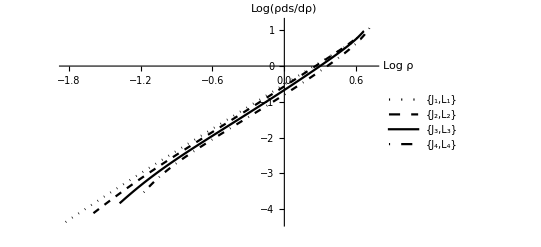

```mathematica
ListLinePlot[{Table[{Log[CS2rho200[s]],Log[.001*CS2rho200[s]/(CS2rho200[s+1]-CS2rho200[s])]},{s,1,921,1}],Table[{Log[CS2rho400[s]],Log[.001*CS2rho400[s]/(CS2rho400[s+1]-CS2rho400[s])]},{s,1,973,1}],Table[{Log[CS2rho600[s]],Log[.001*CS2rho600[s]/(CS2rho600[s+1]-CS2rho600[s])]},{s,1,1038,1}],Table[{Log[CS2rho800[s]],Log[.001*CS2rho800[s]/(CS2rho800[s+1]-CS2rho800[s])]},{s,1,1110,1}]},AxesLabel->{"Log ρ","Log(ρds/dρ)"},PlotStyle->{{Dotted,Black},{Dashed,Black},{Black},{DotDashed,Black}},Ticks->None,PlotLegends->LineLegend[{{{"J_1,L_1"},{"J_2,L_2"},{"J_3,L_3"},{"J_4,L_4"}}},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5]]
```

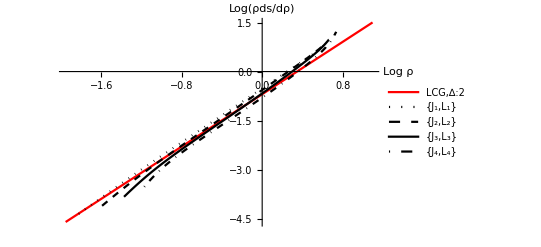

```mathematica
ListLinePlot[{Transpose[{LogRhoalpha2,LogrhoDsDrhoalpha2}],Table[{Log[CS2rho200[s]],Log[.001*CS2rho200[s]/(CS2rho200[s+1]-CS2rho200[s])]},{s,1,921,1}],Table[{Log[CS2rho400[s]],Log[.001*CS2rho400[s]/(CS2rho400[s+1]-CS2rho400[s])]},{s,1,973,1}],Table[{Log[CS2rho600[s]],Log[.001*CS2rho600[s]/(CS2rho600[s+1]-CS2rho600[s])]},{s,1,1038,1}],Table[{Log[CS2rho800[s]],Log[.001*CS2rho800[s]/(CS2rho800[s+1]-CS2rho800[s])]},{s,1,1110,1}]},AxesLabel->{"Log ρ","Log(ρds/dρ)"},PlotStyle->{Red,{Dotted,Black},{Dashed,Black},{Black},{DotDashed,Black}},Ticks->None,PlotLegends->LineLegend[{{"LCG,∆:2",{"J_1,L_1"},{"J_2,L_2"},{"J_3,L_3"},{"J_4,L_4"}}},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5]]
```

```mathematica
LogRhoalpha2=Table[Log[Rho[s,2,2,1]],{s,-0.245,2,0.001}]
LogrhoDsDrhoalpha2=Table[Log[Rho[s,2,2,1]*DsDrho[s,2,2,1]],{s,-0.245,2,0.001}]
```

{-1.95601,-1.86485,-1.78778,-1.72101,-1.66212,-1.60944,-1.56178,-1.51828,-1.47826,-1.4412,-1.40671,-1.37444,-1.34412,-1.31554,-1.28851,-1.26286,-1.23847,-1.21521,-1.19298,-1.1717,-1.15129,-1.13168,-1.11281,-1.09463,-1.07708,-1.06013,-1.04374,-1.02786,-1.01248,-0.99755,-0.983056,-0.968971,-0.955272,-0.941937,-0.92895,-0.916291,-0.903944,-0.891896,-0.88013,-0.868636,-0.857399,-0.84641,-0.835657,-0.82513,-0.81482,-0.804719,-0.794818,-0.785109,-0.775585,-0.766238,-0.757064,-0.748055,-0.739205,-0.730509,-0.721962,-0.713558,-0.705294,-0.697163,-0.689163,-0.681289,-0.673537,-0.665903,-0.658384,-0.650977,-0.643677,-0.636483,-0.629391,-0.622397,-0.615501,-0.608698,-0.601986,-0.595364,-0.588828,-0.582376,-0.576007,-0.569717,-0.563506,-0.557371,-0.55131,-0.545322,-0.539405,-0.533557,-0.527776,-0.522062,-0.516412,-0.510826,-0.505301,-0.499836,-0.494431,-0.489083,-0.483792,-0.478556,-0.473375,-0.468247,-0.463171,-0.458145,-0.45317,-0.448244,-0.443366,-0.438535,-0.43375,-0.429011,-0.424316,-0.419665,-0.415057,-0.41049,-0.405965,-0.401481,-0.397037,-0.392631,-0.388264,-0.383935,-0.379643,-0.375388,-0.371169,-0.366985,-0.362835,-0.35872,-0.354638,-0.35059,-0.346574,-0.34259,-0.338637,-0.334715,-0.330824,-0.326963,-0.323132,-0.319329,-0.315556,-0.311811,-0.308093,-0.304403,-0.30074,-0.297104,-0.293493,-0.289909,-0.286351,-0.282817,-0.279308,-0.275824,-0.272364,-0.268927,-0.265514,-0.262124,-0.258757,-0.255413,-0.252091,-0.24879,-0.245511,-0.242254,-0.239018,-0.235802,-0.232608,-0.229433,-0.226278,-0.223144,-0.220028,-0.216932,-0.213855,-0.210797,-0.207758,-0.204737,-0.201734,-0.198748,-0.195781,-0.192831,-0.189899,-0.186983,-0.184085,-0.181203,-0.178337,-0.175488,-0.172656,-0.169839,-0.167038,-0.164252,-0.161482,-0.158727,-0.155987,-0.153263,-0.150553,-0.147857,-0.145176,-0.142509,-0.139857,-0.137218,-0.134594,-0.131983,-0.129385,-0.126801,-0.124231,-0.121673,-0.119129,-0.116597,-0.114078,-0.111572,-0.109078,-0.106597,-0.104127,-0.10167,-0.0992255,-0.0967924,-0.0943711,-0.0919614,-0.0895633,-0.0871767,-0.0848014,-0.0824373,-0.0800844,-0.0777425,-0.0754114,-0.0730913,-0.0707818,-0.0684829,-0.0661946,-0.0639167,-0.0616491,-0.0593918,-0.0571446,-0.0549074,-0.0526803,-0.050463,-0.0482555,-0.0460576,-0.0438695,-0.0416908,-0.0395216,-0.0373618,-0.0352112,-0.0330699,-0.0309377,-0.0288146,-0.0267004,-0.0245951,-0.0224987,-0.020411,-0.018332,-0.0162616,-0.0141997,-0.0121463,-0.0101014,-0.00806469,-0.00603629,-0.00401609,-0.00200401,0.,0.00199601,0.00398408,0.00596429,0.00793667,0.00990131,0.0118583,0.0138076,0.0157493,0.0176836,0.0196104,0.0215297,0.0234418,0.0253466,0.0272441,0.0291345,0.0310177,0.0328939,0.034763,0.0366252,0.0384805,0.040329,0.0421706,0.0440054,0.0458336,0.0476551,0.04947,0.0512783,0.0530801,0.0548754,0.0566643,0.0584469,0.0602231,0.061993,0.0637567,0.0655141,0.0672654,0.0690106,0.0707498,0.0724829,0.07421,0.0759312,0.0776464,0.0793558,0.0810594,0.0827572,0.0844493,0.0861356,0.0878163,0.0894913,0.0911608,0.0928247,0.094483,0.0961359,0.0977834,0.0994254,0.101062,0.102693,0.104319,0.10594,0.107556,0.109166,0.110771,0.112371,0.113966,0.115556,0.117141,0.11872,0.120295,0.121865,0.12343,0.12499,0.126545,0.128096,0.129641,0.131182,0.132718,0.13425,0.135776,0.137298,0.138816,0.140329,0.141837,0.143341,0.14484,0.146335,0.147825,0.149311,0.150792,0.15227,0.153742,0.155211,0.156675,0.158135,0.15959,0.161042,0.162489,0.163932,0.165371,0.166806,0.168236,0.169663,0.171085,0.172504,0.173918,0.175328,0.176735,0.178137,0.179536,0.180931,0.182322,0.183709,0.185092,0.186471,0.187846,0.189218,0.190586,0.19195,0.193311,0.194668,0.196021,0.197371,0.198716,0.200059,0.201397,0.202733,0.204064,0.205392,0.206717,0.208038,0.209355,0.210669,0.21198,0.213287,0.214591,0.215891,0.217188,0.218482,0.219772,0.221059,0.222343,0.223623,0.2249,0.226174,0.227445,0.228712,0.229977,0.231238,0.232496,0.23375,0.235002,0.23625,0.237496,0.238738,0.239977,0.241213,0.242446,0.243676,0.244903,0.246127,0.247348,0.248566,0.249781,0.250993,0.252203,0.253409,0.254612,0.255813,0.25701,0.258205,0.259397,0.260586,0.261772,0.262956,0.264136,0.265314,0.266489,0.267662,0.268831,0.269998,0.271162,0.272324,0.273482,0.274638,0.275792,0.276943,0.278091,0.279236,0.280379,0.281519,0.282657,0.283792,0.284924,0.286054,0.287182,0.288307,0.289429,0.290549,0.291666,0.292781,0.293893,0.295003,0.296111,0.297216,0.298318,0.299418,0.300516,0.301611,0.302704,0.303795,0.304883,0.305969,0.307052,0.308133,0.309212,0.310288,0.311362,0.312434,0.313504,0.314571,0.315636,0.316699,0.317759,0.318817,0.319873,0.320927,0.321978,0.323028,0.324075,0.32512,0.326163,0.327203,0.328242,0.329278,0.330312,0.331344,0.332374,0.333402,0.334427,0.335451,0.336472,0.337492,0.338509,0.339524,0.340537,0.341548,0.342558,0.343565,0.34457,0.345573,0.346574,0.347573,0.34857,0.349565,0.350558,0.351549,0.352538,0.353525,0.35451,0.355494,0.356475,0.357454,0.358432,0.359407,0.360381,0.361353,0.362323,0.363291,0.364257,0.365221,0.366184,0.367145,0.368103,0.36906,0.370015,0.370969,0.37192,0.37287,0.373818,0.374764,0.375708,0.376651,0.377591,0.37853,0.379467,0.380403,0.381337,0.382269,0.383199,0.384127,0.385054,0.385979,0.386903,0.387824,0.388744,0.389662,0.390579,0.391494,0.392407,0.393319,0.394229,0.395137,0.396044,0.396949,0.397852,0.398754,0.399654,0.400552,0.401449,0.402344,0.403238,0.40413,0.40502,0.405909,0.406797,0.407682,0.408567,0.409449,0.41033,0.41121,0.412088,0.412964,0.413839,0.414712,0.415584,0.416455,0.417323,0.418191,0.419056,0.419921,0.420784,0.421645,0.422505,0.423363,0.42422,0.425075,0.425929,0.426782,0.427633,0.428483,0.429331,0.430178,0.431023,0.431867,0.432709,0.43355,0.43439,0.435228,0.436065,0.4369,0.437734,0.438567,0.439398,0.440228,0.441057,0.441884,0.44271,0.443534,0.444357,0.445179,0.445999,0.446818,0.447636,0.448452,0.449267,0.450081,0.450893,0.451704,0.452514,0.453322,0.454129,0.454935,0.45574,0.456543,0.457345,0.458145,0.458945,0.459743,0.46054,0.461335,0.462129,0.462922,0.463714,0.464505,0.465294,0.466082,0.466869,0.467654,0.468439,0.469222,0.470004,0.470784,0.471564,0.472342,0.473119,0.473895,0.474669,0.475443,0.476215,0.476986,0.477756,0.478524,0.479292,0.480058,0.480823,0.481587,0.48235,0.483112,0.483872,0.484631,0.485389,0.486146,0.486902,0.487657,0.488411,0.489163,0.489914,0.490665,0.491414,0.492162,0.492908,0.493654,0.494399,0.495142,0.495885,0.496626,0.497366,0.498105,0.498843,0.49958,0.500316,0.501051,0.501784,0.502517,0.503248,0.503979,0.504708,0.505437,0.506164,0.50689,0.507615,0.508339,0.509063,0.509785,0.510506,0.511225,0.511944,0.512662,0.513379,0.514095,0.51481,0.515523,0.516236,0.516948,0.517659,0.518368,0.519077,0.519785,0.520492,0.521197,0.521902,0.522606,0.523308,0.52401,0.524711,0.525411,0.52611,0.526807,0.527504,0.5282,0.528895,0.529589,0.530282,0.530974,0.531665,0.532355,0.533045,0.533733,0.53442,0.535106,0.535792,0.536476,0.53716,0.537842,0.538524,0.539205,0.539885,0.540563,0.541241,0.541919,0.542595,0.54327,0.543944,0.544618,0.54529,0.545962,0.546632,0.547302,0.547971,0.548639,0.549306,0.549972,0.550638,0.551302,0.551966,0.552628,0.55329,0.553951,0.554611,0.55527,0.555929,0.556586,0.557243,0.557899,0.558553,0.559207,0.559861,0.560513,0.561164,0.561815,0.562465,0.563114,0.563762,0.564409,0.565055,0.565701,0.566346,0.56699,0.567633,0.568275,0.568917,0.569557,0.570197,0.570836,0.571474,0.572111,0.572748,0.573384,0.574019,0.574653,0.575286,0.575919,0.57655,0.577181,0.577811,0.578441,0.579069,0.579697,0.580324,0.58095,0.581575,0.5822,0.582824,0.583447,0.584069,0.584691,0.585311,0.585931,0.586551,0.587169,0.587787,0.588404,0.58902,0.589635,0.59025,0.590864,0.591477,0.592089,0.592701,0.593312,0.593922,0.594531,0.59514,0.595748,0.596355,0.596961,0.597567,0.598172,0.598776,0.59938,0.599982,0.600584,0.601186,0.601786,0.602386,0.602985,0.603584,0.604182,0.604779,0.605375,0.60597,0.606565,0.60716,0.607753,0.608346,0.608938,0.609529,0.61012,0.61071,0.611299,0.611888,0.612476,0.613063,0.613649,0.614235,0.61482,0.615405,0.615989,0.616572,0.617154,0.617736,0.618317,0.618897,0.619477,0.620056,0.620634,0.621212,0.621789,0.622365,0.622941,0.623516,0.624091,0.624664,0.625237,0.62581,0.626381,0.626953,0.627523,0.628093,0.628662,0.62923,0.629798,0.630366,0.630932,0.631498,0.632063,0.632628,0.633192,0.633755,0.634318,0.63488,0.635442,0.636003,0.636563,0.637122,0.637681,0.63824,0.638797,0.639355,0.639911,0.640467,0.641022,0.641577,0.642131,0.642684,0.643237,0.643789,0.644341,0.644892,0.645442,0.645992,0.646541,0.64709,0.647637,0.648185,0.648732,0.649278,0.649823,0.650368,0.650913,0.651456,0.652,0.652542,0.653084,0.653626,0.654166,0.654707,0.655246,0.655785,0.656324,0.656862,0.657399,0.657936,0.658472,0.659008,0.659543,0.660077,0.660611,0.661145,0.661677,0.662209,0.662741,0.663272,0.663803,0.664333,0.664862,0.665391,0.665919,0.666447,0.666974,0.667501,0.668027,0.668552,0.669077,0.669601,0.670125,0.670648,0.671171,0.671693,0.672215,0.672736,0.673257,0.673777,0.674296,0.674815,0.675334,0.675851,0.676369,0.676886,0.677402,0.677918,0.678433,0.678947,0.679462,0.679975,0.680488,0.681001,0.681513,0.682024,0.682535,0.683046,0.683556,0.684065,0.684574,0.685082,0.68559,0.686098,0.686605,0.687111,0.687617,0.688122,0.688627,0.689131,0.689635,0.690138,0.690641,0.691143,0.691645,0.692146,0.692647,0.693147,0.693647,0.694146,0.694645,0.695143,0.695641,0.696138,0.696635,0.697131,0.697627,0.698122,0.698617,0.699111,0.699605,0.700099,0.700591,0.701084,0.701576,0.702067,0.702558,0.703048,0.703538,0.704028,0.704517,0.705005,0.705493,0.705981,0.706468,0.706955,0.707441,0.707927,0.708412,0.708897,0.709381,0.709865,0.710348,0.710831,0.711313,0.711795,0.712277,0.712758,0.713238,0.713718,0.714198,0.714677,0.715156,0.715634,0.716112,0.716589,0.717066,0.717542,0.718018,0.718494,0.718969,0.719443,0.719918,0.720391,0.720865,0.721337,0.72181,0.722282,0.722753,0.723224,0.723695,0.724165,0.724635,0.725104,0.725573,0.726041,0.726509,0.726977,0.727444,0.72791,0.728376,0.728842,0.729308,0.729772,0.730237,0.730701,0.731165,0.731628,0.73209,0.732553,0.733015,0.733476,0.733937,0.734398,0.734858,0.735318,0.735777,0.736236,0.736695,0.737153,0.73761,0.738068,0.738524,0.738981,0.739437,0.739892,0.740348,0.740802,0.741257,0.741711,0.742164,0.742617,0.74307,0.743522,0.743974,0.744425,0.744877,0.745327,0.745777,0.746227,0.746677,0.747126,0.747574,0.748023,0.74847,0.748918,0.749365,0.749812,0.750258,0.750704,0.751149,0.751594,0.752039,0.752483,0.752927,0.75337,0.753813,0.754256,0.754698,0.75514,0.755582,0.756023,0.756464,0.756904,0.757344,0.757783,0.758223,0.758661,0.7591,0.759538,0.759975,0.760413,0.760849,0.761286,0.761722,0.762158,0.762593,0.763028,0.763463,0.763897,0.764331,0.764764,0.765197,0.76563,0.766062,0.766494,0.766926,0.767357,0.767788,0.768219,0.768649,0.769078,0.769508,0.769937,0.770365,0.770794,0.771222,0.771649,0.772076,0.772503,0.772929,0.773356,0.773781,0.774207,0.774632,0.775056,0.77548,0.775904,0.776328,0.776751,0.777174,0.777596,0.778019,0.77844,0.778862,0.779283,0.779703,0.780124,0.780544,0.780963,0.781383,0.781802,0.78222,0.782639,0.783056,0.783474,0.783891,0.784308,0.784724,0.785141,0.785556,0.785972,0.786387,0.786802,0.787216,0.78763,0.788044,0.788457,0.78887,0.789283,0.789695,0.790108,0.790519,0.790931,0.791342,0.791752,0.792163,0.792573,0.792982,0.793392,0.793801,0.794209,0.794618,0.795026,0.795433,0.795841,0.796248,0.796654,0.797061,0.797467,0.797872,0.798278,0.798683,0.799087,0.799492,0.799896,0.800299,0.800703,0.801106,0.801509,0.801911,0.802313,0.802715,0.803116,0.803518,0.803918,0.804319,0.804719,0.805119,0.805518,0.805918,0.806316,0.806715,0.807113,0.807511,0.807909,0.808306,0.808703,0.8091,0.809496,0.809892,0.810288,0.810683,0.811078,0.811473,0.811868,0.812262,0.812656,0.813049,0.813442,0.813835,0.814228,0.81462,0.815012,0.815404,0.815795,0.816186,0.816577,0.816968,0.817358,0.817748,0.818137,0.818527,0.818915,0.819304,0.819692,0.820081,0.820468,0.820856,0.821243,0.82163,0.822016,0.822403,0.822788,0.823174,0.823559,0.823945,0.824329,0.824714,0.825098,0.825482,0.825865,0.826249,0.826632,0.827014,0.827397,0.827779,0.828161,0.828542,0.828924,0.829304,0.829685,0.830066,0.830446,0.830825,0.831205,0.831584,0.831963,0.832342,0.83272,0.833098,0.833476,0.833853,0.834231,0.834608,0.834984,0.835361,0.835737,0.836112,0.836488,0.836863,0.837238,0.837613,0.837987,0.838361,0.838735,0.839109,0.839482,0.839855,0.840228,0.8406,0.840972,0.841344,0.841716,0.842087,0.842458,0.842829,0.843199,0.84357,0.84394,0.844309,0.844679,0.845048,0.845417,0.845785,0.846154,0.846522,0.84689,0.847257,0.847624,0.847991,0.848358,0.848724,0.849091,0.849456,0.849822,0.850187,0.850553,0.850917,0.851282,0.851646,0.85201,0.852374,0.852738,0.853101,0.853464,0.853826,0.854189,0.854551,0.854913,0.855275,0.855636,0.855997,0.856358,0.856719,0.857079,0.857439,0.857799,0.858159,0.858518,0.858877,0.859236,0.859594,0.859953,0.860311,0.860669,0.861026,0.861383,0.86174,0.862097,0.862454,0.86281,0.863166,0.863522,0.863877,0.864232,0.864587,0.864942,0.865297,0.865651,0.866005,0.866358,0.866712,0.867065,0.867418,0.867771,0.868123,0.868476,0.868828,0.869179,0.869531,0.869882,0.870233,0.870584,0.870934,0.871285,0.871635,0.871984,0.872334,0.872683,0.873032,0.873381,0.87373,0.874078,0.874426,0.874774,0.875121,0.875469,0.875816,0.876163,0.876509,0.876856,0.877202,0.877548,0.877893,0.878239,0.878584,0.878929,0.879274,0.879618,0.879962,0.880306,0.88065,0.880994,0.881337,0.88168,0.882023,0.882365,0.882708,0.88305,0.883392,0.883733,0.884075,0.884416,0.884757,0.885098,0.885438,0.885778,0.886118,0.886458,0.886798,0.887137,0.887476,0.887815,0.888154,0.888492,0.88883,0.889168,0.889506,0.889843,0.890181,0.890518,0.890855,0.891191,0.891528,0.891864,0.8922,0.892535,0.892871,0.893206,0.893541,0.893876,0.89421,0.894545,0.894879,0.895213,0.895546,0.89588,0.896213,0.896546,0.896879,0.897211,0.897544,0.897876,0.898208,0.898539,0.898871,0.899202,0.899533,0.899864,0.900194,0.900525,0.900855,0.901185,0.901515,0.901844,0.902173,0.902502,0.902831,0.90316,0.903488,0.903816,0.904144,0.904472,0.9048,0.905127,0.905454,0.905781,0.906108,0.906434,0.90676,0.907087,0.907412,0.907738,0.908063,0.908389,0.908714,0.909038,0.909363,0.909687,0.910011,0.910335,0.910659,0.910983,0.911306,0.911629,0.911952,0.912275,0.912597,0.912919,0.913241,0.913563,0.913885,0.914206,0.914528,0.914849,0.915169,0.91549,0.915811,0.916131,0.916451,0.916771,0.91709,0.917409,0.917729,0.918048,0.918366,0.918685,0.919003,0.919322,0.919639,0.919957,0.920275,0.920592,0.920909,0.921226,0.921543,0.92186,0.922176,0.922492,0.922808,0.923124,0.923439,0.923755,0.92407,0.924385,0.9247,0.925014,0.925329,0.925643,0.925957,0.92627,0.926584,0.926897,0.927211,0.927524,0.927836,0.928149,0.928461,0.928774,0.929086,0.929397,0.929709,0.93002,0.930332,0.930643,0.930954,0.931264,0.931575,0.931885,0.932195,0.932505,0.932815,0.933124,0.933433,0.933743,0.934052,0.93436,0.934669,0.934977,0.935285,0.935593,0.935901,0.936209,0.936516,0.936823,0.93713,0.937437,0.937744,0.93805,0.938357,0.938663,0.938969,0.939274,0.93958,0.939885,0.94019,0.940495,0.9408,0.941105,0.941409,0.941713,0.942017,0.942321,0.942625,0.942928,0.943232,0.943535,0.943838,0.944141,0.944443,0.944745,0.945048,0.94535,0.945652,0.945953,0.946255,0.946556,0.946857,0.947158,0.947459,0.947759,0.94806,0.94836,0.94866,0.94896,0.94926,0.949559,0.949858,0.950157,0.950456,0.950755,0.951054,0.951352,0.95165,0.951948,0.952246,0.952544,0.952842,0.953139,0.953436,0.953733,0.95403,0.954327,0.954623,0.954919,0.955215,0.955511,0.955807,0.956103,0.956398,0.956693,0.956989,0.957283,0.957578,0.957873,0.958167,0.958461,0.958755,0.959049,0.959343,0.959636,0.95993,0.960223,0.960516,0.960809,0.961101,0.961394,0.961686,0.961978,0.96227,0.962562,0.962854,0.963145,0.963436,0.963728,0.964019,0.964309,0.9646,0.96489,0.965181,0.965471,0.965761,0.96605,0.96634,0.96663,0.966919,0.967208,0.967497,0.967786,0.968074,0.968363,0.968651,0.968939,0.969227,0.969515,0.969802,0.97009,0.970377,0.970664,0.970951,0.971238,0.971524,0.971811,0.972097,0.972383,0.972669,0.972955,0.973241,0.973526,0.973811,0.974097,0.974382,0.974666,0.974951,0.975236,0.97552,0.975804,0.976088,0.976372,0.976656,0.976939,0.977223,0.977506,0.977789,0.978072,0.978354,0.978637,0.978919,0.979202,0.979484,0.979766,0.980047,0.980329,0.98061,0.980892,0.981173,0.981454,0.981735,0.982015,0.982296,0.982576,0.982856,0.983136,0.983416,0.983696,0.983976,0.984255,0.984534,0.984813,0.985092,0.985371,0.98565,0.985928,0.986206,0.986485,0.986763,0.987041,0.987318,0.987596,0.987873,0.98815,0.988427,0.988704,0.988981,0.989258,0.989534,0.989811,0.990087,0.990363,0.990639,0.990914,0.99119,0.991465,0.991741,0.992016,0.992291,0.992565,0.99284,0.993115,0.993389,0.993663,0.993937,0.994211,0.994485,0.994758,0.995032,0.995305,0.995578,0.995851,0.996124,0.996397,0.996669,0.996942,0.997214,0.997486,0.997758,0.99803,0.998302,0.998573,0.998845,0.999116,0.999387,0.999658,0.999929,1.0002,1.00047,1.00074,1.00101,1.00128,1.00155,1.00182,1.00209,1.00236,1.00263,1.0029,1.00317,1.00344,1.0037,1.00397,1.00424,1.00451,1.00478,1.00505,1.00531,1.00558,1.00585,1.00612,1.00638,1.00665,1.00692,1.00718,1.00745,1.00772,1.00798,1.00825,1.00852,1.00878,1.00905,1.00931,1.00958,1.00985,1.01011,1.01038,1.01064,1.01091,1.01117,1.01144,1.0117,1.01196,1.01223,1.01249,1.01276,1.01302,1.01328,1.01355,1.01381,1.01407,1.01434,1.0146,1.01486,1.01513,1.01539,1.01565,1.01591,1.01617,1.01644,1.0167,1.01696,1.01722,1.01748,1.01774,1.01801,1.01827,1.01853,1.01879,1.01905,1.01931,1.01957,1.01983,1.02009,1.02035,1.02061,1.02087,1.02113,1.02139,1.02165,1.02191,1.02217,1.02243,1.02268,1.02294,1.0232,1.02346,1.02372,1.02398,1.02423,1.02449,1.02475,1.02501,1.02526,1.02552,1.02578,1.02604,1.02629,1.02655,1.02681,1.02706,1.02732,1.02757,1.02783,1.02809,1.02834,1.0286,1.02885,1.02911,1.02936,1.02962,1.02987,1.03013,1.03038,1.03064,1.03089,1.03115,1.0314,1.03166,1.03191,1.03216,1.03242,1.03267,1.03292,1.03318,1.03343,1.03368,1.03394,1.03419,1.03444,1.0347,1.03495,1.0352,1.03545,1.0357,1.03596,1.03621,1.03646,1.03671,1.03696,1.03721,1.03747,1.03772,1.03797,1.03822,1.03847,1.03872,1.03897,1.03922,1.03947,1.03972,1.03997,1.04022,1.04047,1.04072,1.04097,1.04122,1.04147,1.04172,1.04197,1.04221,1.04246,1.04271,1.04296,1.04321,1.04346,1.0437,1.04395,1.0442,1.04445,1.0447,1.04494,1.04519,1.04544,1.04569,1.04593,1.04618,1.04643,1.04667,1.04692,1.04717,1.04741,1.04766,1.0479,1.04815,1.0484,1.04864,1.04889,1.04913,1.04938,1.04962,1.04987,1.05011,1.05036,1.0506,1.05085,1.05109,1.05133,1.05158,1.05182,1.05207,1.05231,1.05255,1.0528,1.05304,1.05329,1.05353,1.05377,1.05401,1.05426,1.0545,1.05474,1.05499,1.05523,1.05547,1.05571,1.05595,1.0562,1.05644,1.05668,1.05692,1.05716,1.0574,1.05765,1.05789,1.05813,1.05837,1.05861,1.05885,1.05909,1.05933,1.05957,1.05981,1.06005,1.06029,1.06053,1.06077,1.06101,1.06125,1.06149,1.06173,1.06197,1.06221,1.06245,1.06269,1.06292,1.06316,1.0634,1.06364,1.06388,1.06412,1.06435,1.06459,1.06483,1.06507,1.0653,1.06554,1.06578,1.06602,1.06625,1.06649,1.06673,1.06696,1.0672,1.06744,1.06767,1.06791,1.06815,1.06838,1.06862,1.06886,1.06909,1.06933,1.06956,1.0698,1.07003,1.07027,1.0705,1.07074,1.07097,1.07121,1.07144,1.07168,1.07191,1.07215,1.07238,1.07261,1.07285,1.07308,1.07332,1.07355,1.07378,1.07402,1.07425,1.07448,1.07472,1.07495,1.07518,1.07542,1.07565,1.07588,1.07611,1.07635,1.07658,1.07681,1.07704,1.07727,1.07751,1.07774,1.07797,1.0782,1.07843,1.07866,1.0789,1.07913,1.07936,1.07959,1.07982,1.08005,1.08028,1.08051,1.08074,1.08097,1.0812,1.08143,1.08166,1.08189,1.08212,1.08235,1.08258,1.08281,1.08304,1.08327,1.0835,1.08373,1.08396,1.08418,1.08441,1.08464,1.08487,1.0851,1.08533,1.08555,1.08578,1.08601,1.08624,1.08647,1.08669,1.08692,1.08715,1.08738,1.0876,1.08783,1.08806,1.08828,1.08851,1.08874,1.08896,1.08919,1.08942,1.08964,1.08987,1.0901,1.09032,1.09055,1.09077,1.091,1.09122,1.09145,1.09168,1.0919,1.09213,1.09235,1.09258,1.0928,1.09303,1.09325,1.09347,1.0937,1.09392,1.09415,1.09437,1.0946,1.09482,1.09504,1.09527,1.09549,1.09572,1.09594,1.09616,1.09639,1.09661,1.09683,1.09705,1.09728,1.0975,1.09772,1.09795,1.09817,1.09839,1.09861}

{-4.60517,-4.42285,-4.2687,-4.13517,-4.01738,-3.91202,-3.81671,-3.7297,-3.64966,-3.57555,-3.50656,-3.44202,-3.38139,-3.32424,-3.27017,-3.21888,-3.17009,-3.12357,-3.07911,-3.03655,-2.99573,-2.95651,-2.91877,-2.8824,-2.84731,-2.81341,-2.78062,-2.74887,-2.7181,-2.68825,-2.65926,-2.63109,-2.60369,-2.57702,-2.55105,-2.52573,-2.50104,-2.47694,-2.45341,-2.43042,-2.40795,-2.38597,-2.36446,-2.34341,-2.32279,-2.30259,-2.28278,-2.26336,-2.24432,-2.22562,-2.20727,-2.18926,-2.17156,-2.15417,-2.13707,-2.12026,-2.10373,-2.08747,-2.07147,-2.05573,-2.04022,-2.02495,-2.00992,-1.9951,-1.9805,-1.96611,-1.95193,-1.93794,-1.92415,-1.91054,-1.89712,-1.88387,-1.8708,-1.8579,-1.84516,-1.83258,-1.82016,-1.80789,-1.79577,-1.78379,-1.77196,-1.76026,-1.7487,-1.73727,-1.72597,-1.7148,-1.70375,-1.69282,-1.68201,-1.67131,-1.66073,-1.65026,-1.6399,-1.62964,-1.61949,-1.60944,-1.59949,-1.58964,-1.57988,-1.57022,-1.56065,-1.55117,-1.54178,-1.53248,-1.52326,-1.51413,-1.50508,-1.49611,-1.48722,-1.47841,-1.46968,-1.46102,-1.45243,-1.44392,-1.43548,-1.42712,-1.41882,-1.41059,-1.40242,-1.39433,-1.38629,-1.37833,-1.37042,-1.36258,-1.3548,-1.34707,-1.33941,-1.33181,-1.32426,-1.31677,-1.30933,-1.30195,-1.29463,-1.28735,-1.28013,-1.27297,-1.26585,-1.25878,-1.25176,-1.24479,-1.23787,-1.231,-1.22418,-1.2174,-1.21066,-1.20397,-1.19733,-1.19073,-1.18417,-1.17766,-1.17118,-1.16475,-1.15836,-1.15201,-1.1457,-1.13943,-1.1332,-1.12701,-1.12086,-1.11474,-1.10866,-1.10262,-1.09661,-1.09064,-1.08471,-1.07881,-1.07294,-1.06711,-1.06132,-1.05555,-1.04982,-1.04412,-1.03846,-1.03282,-1.02722,-1.02165,-1.01611,-1.0106,-1.00512,-0.999672,-0.994252,-0.988861,-0.983499,-0.978166,-0.972861,-0.967584,-0.962335,-0.957113,-0.951918,-0.94675,-0.941609,-0.936493,-0.931404,-0.926341,-0.921303,-0.916291,-0.911303,-0.90634,-0.901402,-0.896488,-0.891598,-0.886732,-0.881889,-0.87707,-0.872274,-0.867501,-0.86275,-0.858022,-0.853316,-0.848632,-0.84397,-0.83933,-0.834711,-0.830113,-0.825536,-0.820981,-0.816445,-0.811931,-0.807436,-0.802962,-0.798508,-0.794073,-0.789658,-0.785262,-0.780886,-0.776529,-0.77219,-0.767871,-0.76357,-0.759287,-0.755023,-0.750776,-0.746548,-0.742337,-0.738145,-0.733969,-0.729811,-0.72567,-0.721547,-0.71744,-0.71335,-0.709277,-0.70522,-0.701179,-0.697155,-0.693147,-0.689155,-0.685179,-0.681219,-0.677274,-0.673345,-0.669431,-0.665532,-0.661649,-0.65778,-0.653926,-0.650088,-0.646264,-0.642454,-0.638659,-0.634878,-0.631112,-0.627359,-0.623621,-0.619897,-0.616186,-0.612489,-0.608806,-0.605136,-0.60148,-0.597837,-0.594207,-0.590591,-0.586987,-0.583396,-0.579818,-0.576253,-0.572701,-0.569161,-0.565634,-0.562119,-0.558616,-0.555126,-0.551648,-0.548181,-0.544727,-0.541285,-0.537854,-0.534435,-0.531028,-0.527633,-0.524249,-0.520876,-0.517515,-0.514165,-0.510826,-0.507498,-0.504181,-0.500875,-0.49758,-0.494296,-0.491023,-0.48776,-0.484508,-0.481267,-0.478036,-0.474815,-0.471605,-0.468405,-0.465215,-0.462035,-0.458866,-0.455706,-0.452557,-0.449417,-0.446287,-0.443167,-0.440057,-0.436956,-0.433865,-0.430783,-0.427711,-0.424648,-0.421594,-0.41855,-0.415515,-0.41249,-0.409473,-0.406466,-0.403467,-0.400478,-0.397497,-0.394525,-0.391562,-0.388608,-0.385662,-0.382726,-0.379797,-0.376878,-0.373966,-0.371064,-0.368169,-0.365283,-0.362406,-0.359536,-0.356675,-0.353822,-0.350977,-0.34814,-0.345311,-0.34249,-0.339677,-0.336872,-0.334075,-0.331286,-0.328504,-0.32573,-0.322964,-0.320205,-0.317454,-0.314711,-0.311975,-0.309246,-0.306525,-0.303811,-0.301105,-0.298406,-0.295714,-0.29303,-0.290352,-0.287682,-0.285019,-0.282363,-0.279714,-0.277072,-0.274437,-0.271809,-0.269187,-0.266573,-0.263966,-0.261365,-0.258771,-0.256183,-0.253603,-0.251029,-0.248461,-0.245901,-0.243346,-0.240798,-0.238257,-0.235722,-0.233194,-0.230672,-0.228156,-0.225647,-0.223144,-0.220647,-0.218156,-0.215672,-0.213193,-0.210721,-0.208255,-0.205795,-0.203341,-0.200893,-0.198451,-0.196015,-0.193585,-0.191161,-0.188742,-0.18633,-0.183923,-0.181522,-0.179127,-0.176737,-0.174353,-0.171975,-0.169603,-0.167236,-0.164875,-0.162519,-0.160169,-0.157824,-0.155485,-0.153151,-0.150823,-0.1485,-0.146183,-0.14387,-0.141564,-0.139262,-0.136966,-0.134675,-0.132389,-0.130109,-0.127833,-0.125563,-0.123298,-0.121038,-0.118784,-0.116534,-0.114289,-0.11205,-0.109815,-0.107585,-0.105361,-0.103141,-0.100926,-0.098716,-0.0965109,-0.0943107,-0.0921153,-0.0899247,-0.0877389,-0.0855579,-0.0833816,-0.0812101,-0.0790432,-0.076881,-0.0747235,-0.0725707,-0.0704225,-0.0682788,-0.0661398,-0.0640053,-0.0618754,-0.05975,-0.0576291,-0.0555127,-0.0534008,-0.0512933,-0.0491902,-0.0470916,-0.0449974,-0.0429075,-0.040822,-0.0387408,-0.036664,-0.0345914,-0.0325232,-0.0304592,-0.0283995,-0.026344,-0.0242927,-0.0222456,-0.0202027,-0.018164,-0.0161294,-0.0140989,-0.0120726,-0.0100503,-0.00803217,-0.00601807,-0.00400802,-0.002002,0.,0.001998,0.00399202,0.00598207,0.00796817,0.00995033,0.0119286,0.0139029,0.0158733,0.0178399,0.0198026,0.0217615,0.0237165,0.0256677,0.0276152,0.0295588,0.0314987,0.0334348,0.0353671,0.0372958,0.0392207,0.0411419,0.0430595,0.0449734,0.0468836,0.0487902,0.0506931,0.0525925,0.0544882,0.0563803,0.0582689,0.0601539,0.0620354,0.0639133,0.0657877,0.0676586,0.0695261,0.07139,0.0732505,0.0751075,0.076961,0.0788112,0.0806579,0.0825012,0.0843411,0.0861777,0.0880109,0.0898407,0.0916672,0.0934903,0.0953102,0.0971267,0.0989399,0.10075,0.102557,0.10436,0.10616,0.107957,0.109751,0.111541,0.113329,0.115113,0.116894,0.118672,0.120446,0.122218,0.123986,0.125751,0.127513,0.129272,0.131028,0.132781,0.134531,0.136278,0.138021,0.139762,0.1415,0.143234,0.144966,0.146694,0.14842,0.150143,0.151862,0.153579,0.155293,0.157004,0.158712,0.160417,0.162119,0.163818,0.165514,0.167208,0.168899,0.170586,0.172271,0.173953,0.175633,0.177309,0.178983,0.180653,0.182322,0.183987,0.185649,0.187309,0.188966,0.19062,0.192272,0.193921,0.195567,0.19721,0.198851,0.200489,0.202124,0.203757,0.205387,0.207014,0.208639,0.210261,0.21188,0.213497,0.215111,0.216723,0.218332,0.219938,0.221542,0.223144,0.224742,0.226338,0.227932,0.229523,0.231112,0.232698,0.234281,0.235862,0.237441,0.239017,0.24059,0.242162,0.24373,0.245296,0.24686,0.248421,0.24998,0.251537,0.253091,0.254642,0.256191,0.257738,0.259283,0.260825,0.262364,0.263902,0.265436,0.266969,0.268499,0.270027,0.271553,0.273076,0.274597,0.276115,0.277632,0.279146,0.280657,0.282167,0.283674,0.285179,0.286682,0.288182,0.28968,0.291176,0.29267,0.294161,0.29565,0.297137,0.298622,0.300105,0.301585,0.303063,0.304539,0.306013,0.307485,0.308954,0.310422,0.311887,0.31335,0.314811,0.31627,0.317726,0.319181,0.320633,0.322083,0.323532,0.324978,0.326422,0.327864,0.329304,0.330742,0.332177,0.333611,0.335043,0.336472,0.3379,0.339325,0.340749,0.34217,0.34359,0.345007,0.346423,0.347836,0.349247,0.350657,0.352064,0.35347,0.354873,0.356275,0.357674,0.359072,0.360468,0.361861,0.363253,0.364643,0.366031,0.367417,0.368801,0.370183,0.371564,0.372942,0.374318,0.375693,0.377066,0.378436,0.379805,0.381172,0.382538,0.383901,0.385262,0.386622,0.38798,0.389336,0.39069,0.392042,0.393393,0.394741,0.396088,0.397433,0.398776,0.400118,0.401457,0.402795,0.404131,0.405465,0.406798,0.408128,0.409457,0.410784,0.41211,0.413433,0.414755,0.416075,0.417394,0.41871,0.420025,0.421338,0.42265,0.42396,0.425268,0.426574,0.427879,0.429182,0.430483,0.431782,0.43308,0.434376,0.435671,0.436964,0.438255,0.439544,0.440832,0.442118,0.443403,0.444686,0.445967,0.447247,0.448525,0.449801,0.451076,0.452349,0.45362,0.45489,0.456158,0.457425,0.45869,0.459953,0.461215,0.462475,0.463734,0.464991,0.466247,0.4675,0.468753,0.470004,0.471253,0.472501,0.473747,0.474991,0.476234,0.477476,0.478716,0.479954,0.481191,0.482426,0.48366,0.484892,0.486123,0.487352,0.48858,0.489806,0.491031,0.492254,0.493476,0.494696,0.495915,0.497132,0.498348,0.499562,0.500775,0.501987,0.503197,0.504405,0.505612,0.506818,0.508022,0.509224,0.510426,0.511625,0.512824,0.514021,0.515216,0.51641,0.517603,0.518794,0.519984,0.521172,0.522359,0.523544,0.524729,0.525911,0.527093,0.528273,0.529451,0.530628,0.531804,0.532978,0.534151,0.535323,0.536493,0.537662,0.53883,0.539996,0.541161,0.542324,0.543486,0.544647,0.545807,0.546965,0.548121,0.549277,0.550431,0.551584,0.552735,0.553885,0.555034,0.556181,0.557327,0.558472,0.559616,0.560758,0.561899,0.563038,0.564177,0.565314,0.56645,0.567584,0.568717,0.569849,0.57098,0.572109,0.573237,0.574364,0.575489,0.576613,0.577736,0.578858,0.579978,0.581098,0.582216,0.583332,0.584448,0.585562,0.586675,0.587787,0.588897,0.590006,0.591114,0.592221,0.593327,0.594431,0.595534,0.596636,0.597737,0.598837,0.599935,0.601032,0.602128,0.603222,0.604316,0.605408,0.606499,0.607589,0.608678,0.609766,0.610852,0.611937,0.613021,0.614104,0.615186,0.616266,0.617345,0.618424,0.619501,0.620576,0.621651,0.622725,0.623797,0.624868,0.625938,0.627007,0.628075,0.629142,0.630207,0.631272,0.632335,0.633397,0.634458,0.635518,0.636577,0.637634,0.638691,0.639746,0.640801,0.641854,0.642906,0.643957,0.645007,0.646056,0.647103,0.64815,0.649195,0.65024,0.651283,0.652325,0.653366,0.654406,0.655445,0.656483,0.65752,0.658556,0.65959,0.660624,0.661657,0.662688,0.663718,0.664748,0.665776,0.666803,0.667829,0.668854,0.669879,0.670902,0.671924,0.672944,0.673964,0.674983,0.676001,0.677018,0.678034,0.679048,0.680062,0.681075,0.682086,0.683097,0.684106,0.685115,0.686123,0.687129,0.688135,0.689139,0.690143,0.691145,0.692147,0.693147,0.694147,0.695145,0.696143,0.697139,0.698135,0.699129,0.700123,0.701115,0.702107,0.703098,0.704087,0.705076,0.706063,0.70705,0.708036,0.709021,0.710004,0.710987,0.711969,0.71295,0.71393,0.714909,0.715887,0.716864,0.71784,0.718815,0.719789,0.720762,0.721735,0.722706,0.723676,0.724646,0.725614,0.726582,0.727549,0.728514,0.729479,0.730443,0.731406,0.732368,0.733329,0.734289,0.735248,0.736207,0.737164,0.738121,0.739076,0.740031,0.740985,0.741937,0.742889,0.74384,0.74479,0.74574,0.746688,0.747635,0.748582,0.749528,0.750472,0.751416,0.752359,0.753301,0.754242,0.755183,0.756122,0.757061,0.757998,0.758935,0.759871,0.760806,0.76174,0.762673,0.763606,0.764537,0.765468,0.766398,0.767327,0.768255,0.769182,0.770108,0.771034,0.771958,0.772882,0.773805,0.774727,0.775648,0.776569,0.777488,0.778407,0.779325,0.780242,0.781158,0.782073,0.782988,0.783902,0.784814,0.785726,0.786638,0.787548,0.788457,0.789366,0.790274,0.791181,0.792087,0.792993,0.793897,0.794801,0.795704,0.796606,0.797507,0.798408,0.799307,0.800206,0.801104,0.802002,0.802898,0.803794,0.804689,0.805583,0.806476,0.807368,0.80826,0.809151,0.810041,0.81093,0.811819,0.812706,0.813593,0.814479,0.815365,0.816249,0.817133,0.818016,0.818898,0.81978,0.820661,0.82154,0.82242,0.823298,0.824175,0.825052,0.825928,0.826804,0.827678,0.828552,0.829425,0.830297,0.831168,0.832039,0.832909,0.833778,0.834647,0.835514,0.836381,0.837248,0.838113,0.838978,0.839842,0.840705,0.841567,0.842429,0.84329,0.84415,0.84501,0.845868,0.846726,0.847584,0.84844,0.849296,0.850151,0.851005,0.851859,0.852712,0.853564,0.854415,0.855266,0.856116,0.856965,0.857814,0.858662,0.859509,0.860355,0.861201,0.862046,0.86289,0.863733,0.864576,0.865418,0.86626,0.8671,0.86794,0.86878,0.869618,0.870456,0.871293,0.87213,0.872966,0.873801,0.874635,0.875469,0.876302,0.877134,0.877966,0.878797,0.879627,0.880456,0.881285,0.882113,0.882941,0.883768,0.884594,0.885419,0.886244,0.887068,0.887891,0.888714,0.889536,0.890357,0.891178,0.891998,0.892817,0.893636,0.894454,0.895271,0.896088,0.896904,0.897719,0.898534,0.899348,0.900161,0.900974,0.901786,0.902597,0.903408,0.904218,0.905028,0.905836,0.906644,0.907452,0.908259,0.909065,0.90987,0.910675,0.911479,0.912283,0.913086,0.913888,0.914689,0.91549,0.916291,0.91709,0.917889,0.918688,0.919486,0.920283,0.921079,0.921875,0.92267,0.923465,0.924259,0.925052,0.925845,0.926637,0.927428,0.928219,0.92901,0.929799,0.930588,0.931376,0.932164,0.932951,0.933738,0.934524,0.935309,0.936093,0.936877,0.937661,0.938444,0.939226,0.940007,0.940788,0.941569,0.942348,0.943127,0.943906,0.944684,0.945461,0.946238,0.947014,0.947789,0.948564,0.949339,0.950112,0.950885,0.951658,0.95243,0.953201,0.953972,0.954742,0.955511,0.95628,0.957049,0.957816,0.958584,0.95935,0.960116,0.960882,0.961646,0.962411,0.963174,0.963937,0.9647,0.965462,0.966223,0.966984,0.967744,0.968504,0.969263,0.970021,0.970779,0.971536,0.972293,0.973049,0.973805,0.97456,0.975314,0.976068,0.976821,0.977574,0.978326,0.979078,0.979829,0.980579,0.981329,0.982078,0.982827,0.983575,0.984323,0.98507,0.985817,0.986563,0.987308,0.988053,0.988797,0.989541,0.990284,0.991027,0.991769,0.992511,0.993252,0.993992,0.994732,0.995472,0.99621,0.996949,0.997686,0.998424,0.99916,0.999896,1.00063,1.00137,1.0021,1.00284,1.00357,1.0043,1.00503,1.00577,1.0065,1.00723,1.00796,1.00869,1.00942,1.01015,1.01087,1.0116,1.01233,1.01305,1.01378,1.01451,1.01523,1.01596,1.01668,1.0174,1.01813,1.01885,1.01957,1.02029,1.02101,1.02173,1.02245,1.02317,1.02389,1.02461,1.02532,1.02604,1.02676,1.02747,1.02819,1.0289,1.02962,1.03033,1.03105,1.03176,1.03247,1.03318,1.0339,1.03461,1.03532,1.03603,1.03674,1.03745,1.03815,1.03886,1.03957,1.04028,1.04098,1.04169,1.04239,1.0431,1.0438,1.04451,1.04521,1.04591,1.04662,1.04732,1.04802,1.04872,1.04942,1.05012,1.05082,1.05152,1.05222,1.05292,1.05361,1.05431,1.05501,1.0557,1.0564,1.0571,1.05779,1.05848,1.05918,1.05987,1.06056,1.06126,1.06195,1.06264,1.06333,1.06402,1.06471,1.0654,1.06609,1.06678,1.06747,1.06815,1.06884,1.06953,1.07021,1.0709,1.07158,1.07227,1.07295,1.07364,1.07432,1.075,1.07568,1.07637,1.07705,1.07773,1.07841,1.07909,1.07977,1.08045,1.08113,1.08181,1.08248,1.08316,1.08384,1.08451,1.08519,1.08586,1.08654,1.08721,1.08789,1.08856,1.08924,1.08991,1.09058,1.09125,1.09192,1.09259,1.09326,1.09393,1.0946,1.09527,1.09594,1.09661,1.09728,1.09795,1.09861,1.09928,1.09994,1.10061,1.10128,1.10194,1.1026,1.10327,1.10393,1.10459,1.10526,1.10592,1.10658,1.10724,1.1079,1.10856,1.10922,1.10988,1.11054,1.1112,1.11186,1.11252,1.11317,1.11383,1.11449,1.11514,1.1158,1.11645,1.11711,1.11776,1.11841,1.11907,1.11972,1.12037,1.12103,1.12168,1.12233,1.12298,1.12363,1.12428,1.12493,1.12558,1.12623,1.12688,1.12752,1.12817,1.12882,1.12946,1.13011,1.13076,1.1314,1.13205,1.13269,1.13334,1.13398,1.13462,1.13527,1.13591,1.13655,1.13719,1.13783,1.13847,1.13911,1.13975,1.14039,1.14103,1.14167,1.14231,1.14295,1.14359,1.14422,1.14486,1.1455,1.14613,1.14677,1.1474,1.14804,1.14867,1.14931,1.14994,1.15057,1.1512,1.15184,1.15247,1.1531,1.15373,1.15436,1.15499,1.15562,1.15625,1.15688,1.15751,1.15814,1.15877,1.15939,1.16002,1.16065,1.16127,1.1619,1.16253,1.16315,1.16378,1.1644,1.16502,1.16565,1.16627,1.16689,1.16752,1.16814,1.16876,1.16938,1.17,1.17062,1.17124,1.17186,1.17248,1.1731,1.17372,1.17434,1.17496,1.17557,1.17619,1.17681,1.17742,1.17804,1.17865,1.17927,1.17989,1.1805,1.18111,1.18173,1.18234,1.18295,1.18357,1.18418,1.18479,1.1854,1.18601,1.18662,1.18723,1.18784,1.18845,1.18906,1.18967,1.19028,1.19089,1.1915,1.1921,1.19271,1.19332,1.19392,1.19453,1.19513,1.19574,1.19634,1.19695,1.19755,1.19816,1.19876,1.19936,1.19996,1.20057,1.20117,1.20177,1.20237,1.20297,1.20357,1.20417,1.20477,1.20537,1.20597,1.20657,1.20717,1.20777,1.20836,1.20896,1.20956,1.21015,1.21075,1.21135,1.21194,1.21254,1.21313,1.21373,1.21432,1.21491,1.21551,1.2161,1.21669,1.21728,1.21788,1.21847,1.21906,1.21965,1.22024,1.22083,1.22142,1.22201,1.2226,1.22319,1.22378,1.22436,1.22495,1.22554,1.22613,1.22671,1.2273,1.22788,1.22847,1.22906,1.22964,1.23023,1.23081,1.23139,1.23198,1.23256,1.23314,1.23373,1.23431,1.23489,1.23547,1.23605,1.23663,1.23721,1.23779,1.23837,1.23895,1.23953,1.24011,1.24069,1.24127,1.24185,1.24242,1.243,1.24358,1.24415,1.24473,1.24531,1.24588,1.24646,1.24703,1.24761,1.24818,1.24875,1.24933,1.2499,1.25047,1.25105,1.25162,1.25219,1.25276,1.25333,1.25391,1.25448,1.25505,1.25562,1.25619,1.25675,1.25732,1.25789,1.25846,1.25903,1.2596,1.26016,1.26073,1.2613,1.26186,1.26243,1.263,1.26356,1.26413,1.26469,1.26526,1.26582,1.26638,1.26695,1.26751,1.26807,1.26864,1.2692,1.26976,1.27032,1.27088,1.27144,1.27201,1.27257,1.27313,1.27369,1.27424,1.2748,1.27536,1.27592,1.27648,1.27704,1.27759,1.27815,1.27871,1.27927,1.27982,1.28038,1.28093,1.28149,1.28204,1.2826,1.28315,1.28371,1.28426,1.28482,1.28537,1.28592,1.28647,1.28703,1.28758,1.28813,1.28868,1.28923,1.28978,1.29033,1.29088,1.29143,1.29198,1.29253,1.29308,1.29363,1.29418,1.29473,1.29527,1.29582,1.29637,1.29692,1.29746,1.29801,1.29856,1.2991,1.29965,1.30019,1.30074,1.30128,1.30183,1.30237,1.30291,1.30346,1.304,1.30454,1.30508,1.30563,1.30617,1.30671,1.30725,1.30779,1.30833,1.30887,1.30941,1.30995,1.31049,1.31103,1.31157,1.31211,1.31265,1.31319,1.31372,1.31426,1.3148,1.31534,1.31587,1.31641,1.31694,1.31748,1.31802,1.31855,1.31909,1.31962,1.32015,1.32069,1.32122,1.32176,1.32229,1.32282,1.32335,1.32389,1.32442,1.32495,1.32548,1.32601,1.32654,1.32708,1.32761,1.32814,1.32867,1.32919,1.32972,1.33025,1.33078,1.33131,1.33184,1.33237,1.33289,1.33342,1.33395,1.33447,1.335,1.33553,1.33605,1.33658,1.3371,1.33763,1.33815,1.33868,1.3392,1.33973,1.34025,1.34077,1.3413,1.34182,1.34234,1.34286,1.34339,1.34391,1.34443,1.34495,1.34547,1.34599,1.34651,1.34703,1.34755,1.34807,1.34859,1.34911,1.34963,1.35015,1.35067,1.35119,1.3517,1.35222,1.35274,1.35325,1.35377,1.35429,1.3548,1.35532,1.35584,1.35635,1.35687,1.35738,1.35789,1.35841,1.35892,1.35944,1.35995,1.36046,1.36098,1.36149,1.362,1.36251,1.36303,1.36354,1.36405,1.36456,1.36507,1.36558,1.36609,1.3666,1.36711,1.36762,1.36813,1.36864,1.36915,1.36966,1.37016,1.37067,1.37118,1.37169,1.3722,1.3727,1.37321,1.37372,1.37422,1.37473,1.37523,1.37574,1.37624,1.37675,1.37725,1.37776,1.37826,1.37877,1.37927,1.37977,1.38028,1.38078,1.38128,1.38178,1.38229,1.38279,1.38329,1.38379,1.38429,1.38479,1.38529,1.38579,1.38629,1.38679,1.38729,1.38779,1.38829,1.38879,1.38929,1.38979,1.39029,1.39078,1.39128,1.39178,1.39228,1.39277,1.39327,1.39377,1.39426,1.39476,1.39525,1.39575,1.39624,1.39674,1.39723,1.39773,1.39822,1.39872,1.39921,1.3997,1.4002,1.40069,1.40118,1.40168,1.40217,1.40266,1.40315,1.40364,1.40413,1.40463,1.40512,1.40561,1.4061,1.40659,1.40708,1.40757,1.40806,1.40854,1.40903,1.40952,1.41001,1.4105,1.41099,1.41147,1.41196,1.41245,1.41294,1.41342,1.41391,1.4144,1.41488,1.41537,1.41585,1.41634,1.41682,1.41731,1.41779,1.41828,1.41876,1.41925,1.41973,1.42021,1.4207,1.42118,1.42166,1.42214,1.42263,1.42311,1.42359,1.42407,1.42455,1.42503,1.42552,1.426,1.42648,1.42696,1.42744,1.42792,1.4284,1.42887,1.42935,1.42983,1.43031,1.43079,1.43127,1.43175,1.43222,1.4327,1.43318,1.43365,1.43413,1.43461,1.43508,1.43556,1.43604,1.43651,1.43699,1.43746,1.43794,1.43841,1.43889,1.43936,1.43984,1.44031,1.44078,1.44126,1.44173,1.4422,1.44267,1.44315,1.44362,1.44409,1.44456,1.44503,1.44551,1.44598,1.44645,1.44692,1.44739,1.44786,1.44833,1.4488,1.44927,1.44974,1.45021,1.45068,1.45115,1.45161,1.45208,1.45255,1.45302,1.45349,1.45395,1.45442,1.45489,1.45535,1.45582,1.45629,1.45675,1.45722,1.45768,1.45815,1.45862,1.45908,1.45954,1.46001,1.46047,1.46094,1.4614,1.46187,1.46233,1.46279,1.46326,1.46372,1.46418,1.46464,1.46511,1.46557,1.46603,1.46649,1.46695,1.46741,1.46787,1.46834,1.4688,1.46926,1.46972,1.47018,1.47064,1.47109,1.47155,1.47201,1.47247,1.47293,1.47339,1.47385,1.47431,1.47476,1.47522,1.47568,1.47614,1.47659,1.47705,1.47751,1.47796,1.47842,1.47887,1.47933,1.47978,1.48024,1.4807,1.48115,1.4816,1.48206,1.48251,1.48297,1.48342,1.48387,1.48433,1.48478,1.48523,1.48569,1.48614,1.48659,1.48704,1.4875,1.48795,1.4884,1.48885,1.4893,1.48975,1.4902,1.49065,1.4911,1.49155,1.492,1.49245,1.4929,1.49335,1.4938,1.49425,1.4947,1.49515,1.4956,1.49605,1.49649,1.49694,1.49739,1.49784,1.49828,1.49873,1.49918,1.49962,1.50007,1.50052,1.50096,1.50141,1.50185,1.5023,1.50274,1.50319,1.50363,1.50408}

## Figure 7

(a)

## Set up

```mathematica
kernelcodeHP="
#define min 0
#define max 1
#define uuu 0
#define vvv 1
#define sign1 1
#define h 0.001
#define n 1201
#define n_j 302


#define inidxdu1 (tu1)
#define inidxdu2 (0)
#define inidxdu3 (tu2)
#define inidxdv1 (0)
#define inidxdv2 (tv1)
#define inidxdv3 (tv2)

#define inid2xdu21 (dtu1)
#define inid2xdu22 (0)
#define inid2xdu23 (dtu2)
#define inid2xdv21 (0)
#define inid2xdv22 (dtv1)
#define inid2xdv23 (dtv2)
#define inid2xdudv1 (0)
#define inid2xdudv2 (0)
#define inid2xdudv3 (0)

#define inid3xdu31 (d2tu1)
#define inid3xdu32 (0)
#define inid3xdu33 (d2tu2)
#define inid3xdv31 (0)
#define inid3xdv32 (d2tv1)
#define inid3xdv33 (d2tv2)
#define inid3xdu2dv1 (0)
#define inid3xdu2dv2 (0)
#define inid3xdu2dv3 (0)
#define inid3xdudv21 (0)
#define inid3xdudv22 (0)
#define inid3xdudv23 (0)



#define repiniSurNorvec iniSurNorvec(xu1,xu2,tu1,tu2,xv1,xv2,tv1,tv2,normv_C)
#define repiniDSurNvDu iniDSurNvDu(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,dnormvdu_C)
#define repiniDSurNvDv iniDSurNvDv(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,dnormvdv_C)
#define repiniScalarSurNor iniScalarSurNor(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,Scal)
#define repinicoefE inicoefE(xu1,xu2,tu1,tu2,xv1,xv2,tv1,tv2)
#define repiniDEDu iniDEDu(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniDEDv iniDEDv(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repinicoefF inicoefF(xu1,xu2,tu1,tu2,xv1,xv2,tv1,tv2)
#define repiniDFDu iniDFDu(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniDFDv iniDFDv(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repinicoefG inicoefG(xu1,xu2,tu1,tu2,xv1,xv2,tv1,tv2)
#define repiniDGDu iniDGDu(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniDGDv iniDGDv(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repinicoefL inicoefL(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repinicoefM inicoefM(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repinicoefN inicoefN(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniGaussCurva iniGaussCurva(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniMeanCurva iniMeanCurva(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniMaxPrinci iniMaxPrinci(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniMinPrinci iniMinPrinci(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2)
#define repiniPrinci iniPrinci(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)

#define repiniDcoefL_2 iniDcoefL_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,CoeffL)
#define repiniDcoefM_2 iniDcoefM_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,CoeffM)
#define repiniDcoefN_2 iniDcoefN_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,CoeffN)
#define repiniDGaussCurva_2 iniDGaussCurva_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,GCurva)
#define repiniDMeanCurva_2 iniDMeanCurva_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,MCurva)
#define repiniDPrinci_2 iniDPrinci_2(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,PCurva)
#define repiniEta iniEta(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniMiu  iniMiu(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDuDs iniDuDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDvDs iniDvDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDEDs iniDEDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDFDs iniDFDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDGDs iniDGDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDLDs iniDLDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repiniDMDs iniDMDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repiniDNDs iniDNDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repiniDPrinciDs iniDPrinciDs(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)
#define repiniDvDt iniDvDt(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDuDt iniDuDt(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum)
#define repiniDSurDs iniDSurDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum,tangv)
#define repiniSurNor iniSurNor(xu1,xu2,tu1,tu2,xv1,xv2,tv1,tv2,Snor_C)
#define repiniBinormalSur iniBinormalSur(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum,binormv_C)
#define repiniAlp1 iniAlp1(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum,Alp1_C)
#define repiniBeta1 iniBeta1(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum)


#define opt1 (float xu1,float xu2,float tu1,float tu2,float xv1,float xv2,float tv1,float tv2,float normv_C[])
#define opt2 (float xu1,float xu2,float tu1,float tu2,float xv1,float xv2,float tv1,float tv2)
#define opt3 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2)
#define opt4 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,mint optimum)
 #define opt5 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,mint optimum,float tangv_C[])
#define opt6 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float dnormv_C[])
#define opt7 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float Scal[])
#define opt8 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,float coeff[])
#define opt9 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,mint optimum,float coeff[])
#define opt10 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,mint optimum)
#define opt11 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,mint optimum,float Alph_C[])
#define opt12 (float xu1,float xu2,float tu1,float tu2,float xv1,float xv2,float tv1,float tv2,float Snor_C[])
#define opt13 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,mint optimum,float binormv_C[])
#define opt14 (float xu1,float xu2,float tu1,float tu2,float dtu1,float dtu2,float d2tu1,float d2tu2,float xv1,float xv2,float tv1,float tv2,float dtv1,float dtv2,float d2tv1,float d2tv2,mint optimum,float x[])




__device__ void iniSurNorvec opt1 
{
	normv_C[0] =inidxdu2*inidxdv3-inidxdu3*inidxdv2; 
	normv_C[1] =inidxdu3*inidxdv1-inidxdu1*inidxdv3;
	normv_C[2] =inidxdu1*inidxdv2-inidxdu2*inidxdv1; 
}
__device__ void iniDSurNvDu opt6
{
	dnormv_C[0] =(inid2xdu22*inidxdv3-inid2xdu23*inidxdv2)+(inidxdu2*inid2xdudv3-inidxdu3*inid2xdudv2); 
	dnormv_C[1] =(inid2xdu23*inidxdv1-inid2xdu21*inidxdv3)+(inidxdu3*inid2xdudv1-inidxdu1*inid2xdudv3);
	dnormv_C[2] =(inid2xdu21*inidxdv2-inid2xdu22*inidxdv1)+(inidxdu1*inid2xdudv2-inidxdu2*inid2xdudv1); 
}
__device__ void iniDSurNvDv opt6
{
	dnormv_C[0] =(inid2xdudv2*inidxdv3-inid2xdudv3*inidxdv2)+(inidxdu2*inid2xdv23-inidxdu3*inid2xdv22); 
	dnormv_C[1] =(inid2xdudv3*inidxdv1-inid2xdudv1*inidxdv3)+(inidxdu3*inid2xdv21-inidxdu1*inid2xdv23); 
	dnormv_C[2] =(inid2xdudv1*inidxdv2-inid2xdudv2*inidxdv1)+(inidxdu1*inid2xdv22-inidxdu2*inid2xdv21); 
}

__device__ void iniScalarSurNor opt7
{
float ScalSNor,DScalSNorDu,DScalSNorDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];

repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;


ScalSNor = sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
DScalSNorDu = (normv_C[0]*dnormvdu_C[0]+normv_C[1]*dnormvdu_C[1]+normv_C[2]*dnormvdu_C[2])/ScalSNor;
DScalSNorDv = (normv_C[0]*dnormvdv_C[0]+normv_C[1]*dnormvdv_C[1]+normv_C[2]*dnormvdv_C[2])/ScalSNor;


Scal[0] = ScalSNor;
Scal[1] = DScalSNorDu;
Scal[2] = DScalSNorDv;
}

__device__ float inicoefE opt2
{
	return inidxdu1*inidxdu1+inidxdu2*inidxdu2+inidxdu3*inidxdu3; 
}
__device__ float iniDEDu opt3
{
	return 2*(inidxdu1*inid2xdu21+inidxdu2*inid2xdu22+inidxdu3*inid2xdu23);
}
__device__ float iniDEDv opt3
{
	return 2*(inidxdu1*inid2xdudv1+inidxdu2*inid2xdudv2+inidxdu3*inid2xdudv3);
}

 
__device__ float inicoefF opt2
{ 
	return (inidxdu1*inidxdv1+inidxdu2*inidxdv2+inidxdu3*inidxdv3); 
}
__device__ float iniDFDu opt3
{ 
	return inidxdv1*inid2xdu21+inidxdv2*inid2xdu22+inidxdv3*inid2xdu23 + inidxdu1*inid2xdudv1+inidxdu2*inid2xdudv2+inidxdu3*inid2xdudv3;
}
__device__ float iniDFDv opt3
{ 
	return inidxdv1*inid2xdudv1+inidxdv2*inid2xdudv2+inidxdv3*inid2xdudv3 + inidxdu1*inid2xdv21+inidxdu2*inid2xdv22+inidxdu3*inid2xdv23;
}

__device__ float inicoefG opt2
{ 
	return inidxdv1*inidxdv1+inidxdv2*inidxdv2+inidxdv3*inidxdv3; 
}
__device__ float iniDGDu opt3
{ 
	return 2*(inidxdv1*inid2xdudv1+inidxdv2*inid2xdudv2+inidxdv3*inid2xdudv3);
}
__device__ float iniDGDv opt3
{ 
	return 2*(inidxdv1*inid2xdv21+inidxdv2*inid2xdv22+inidxdv3*inid2xdv23);
}

__device__ float inicoefL opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdu21+normv_C[1]*inid2xdu22+normv_C[2]*inid2xdu23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float inicoefM opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdudv1+normv_C[1]*inid2xdudv2+normv_C[2]*inid2xdudv3)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float inicoefN opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdv21+normv_C[1]*inid2xdv22+normv_C[2]*inid2xdv23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float iniGaussCurva opt3
{
	return (repinicoefL*repinicoefN-pow(repinicoefM,2))/(repinicoefE*repinicoefG-pow(repinicoefF,2)); 
}
__device__ float iniMeanCurva opt3
{
	return 0.5*(repinicoefE*repinicoefN+repinicoefG*repinicoefL-2*repinicoefF*repinicoefM)/(repinicoefE*repinicoefG-pow(repinicoefF,2));
}
__device__ float iniMaxPrinci opt3
{
	return repiniMeanCurva+sqrt(pow(repiniMeanCurva,2)-repiniGaussCurva); 
}

__device__ float iniMinPrinci opt3
{
	return repiniMeanCurva-sqrt(pow(repiniMeanCurva,2)-repiniGaussCurva); 
}
__device__ float iniPrinci opt4
{ 	
	if(optimum==max) 
	{return repiniMaxPrinci;} 
	else if(optimum==min)
	{return repiniMinPrinci;}
	else
	{return 0;}
}
__device__ void iniDcoefL_2 opt8
{

float CoeL,DCoeLDu,DCoeLDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];

repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;
repiniScalarSurNor;

CoeL = (normv_C[0]*inid2xdu21+normv_C[1]*inid2xdu22+normv_C[2]*inid2xdu23)/Scal[0];
DCoeLDu = ((dnormvdu_C[0]*inid2xdu21+dnormvdu_C[1]*inid2xdu22+dnormvdu_C[2]*inid2xdu23)+(normv_C[0]*inid3xdu31+normv_C[1]*inid3xdu32+normv_C[2]*inid3xdu33)-Scal[1]*CoeL)/Scal[0];
DCoeLDv = ((dnormvdv_C[0]*inid2xdu21+dnormvdv_C[1]*inid2xdu22+dnormvdv_C[2]*inid2xdu23)+(normv_C[0]*inid3xdu2dv1+normv_C[1]*inid3xdu2dv2+normv_C[2]*inid3xdu2dv3)-Scal[2]*CoeL)/Scal[0];

coeff[0] = CoeL;
coeff[1] = DCoeLDu;
coeff[2] = DCoeLDv;

}
__device__ void iniDcoefM_2 opt8
{
float CoeM,DCoeMDu,DCoeMDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];
repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;
repiniScalarSurNor;

CoeM = (normv_C[0]*inid2xdudv1+normv_C[1]*inid2xdudv2+normv_C[2]*inid2xdudv3)/Scal[0];
DCoeMDu = ((dnormvdu_C[0]*inid2xdudv1+dnormvdu_C[1]*inid2xdudv2+dnormvdu_C[2]*inid2xdudv3)+(normv_C[0]*inid3xdu2dv1+normv_C[1]*inid3xdu2dv2+normv_C[2]*inid3xdu2dv3)-Scal[1]*CoeM)/Scal[0];
DCoeMDv = ((dnormvdv_C[0]*inid2xdudv1+dnormvdv_C[1]*inid2xdudv2+dnormvdv_C[2]*inid2xdudv3)+(normv_C[0]*inid3xdudv21+normv_C[1]*inid3xdudv22+normv_C[2]*inid3xdudv23)-Scal[2]*CoeM)/Scal[0];


coeff[0] = CoeM;
coeff[1] = DCoeMDu;
coeff[2] = DCoeMDv;
}
__device__ void iniDcoefN_2 opt8
{
float CoeN,DCoeNDu,DCoeNDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];
repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;
repiniScalarSurNor;

CoeN = (normv_C[0]*inid2xdv21+normv_C[1]*inid2xdv22+normv_C[2]*inid2xdv23)/Scal[0];
DCoeNDu = ((dnormvdu_C[0]*inid2xdv21+dnormvdu_C[1]*inid2xdv22+dnormvdu_C[2]*inid2xdv23)+(normv_C[0]*inid3xdudv21+normv_C[1]*inid3xdudv22+normv_C[2]*inid3xdudv23)-Scal[1]*CoeN)/Scal[0];
DCoeNDv = ((dnormvdv_C[0]*inid2xdv21+dnormvdv_C[1]*inid2xdv22+dnormvdv_C[2]*inid2xdv23)+(normv_C[0]*inid3xdv31+normv_C[1]*inid3xdv32+normv_C[2]*inid3xdv33)-Scal[2]*CoeN)/Scal[0];

coeff[0] = CoeN;
coeff[1] = DCoeNDu;
coeff[2] = DCoeNDv;

}
__device__ void iniDGaussCurva_2 opt8 
{
float GCurv,DGCurvDu,DGCurvDv;
float CoeffL[3];
float CoeffM[3];
float CoeffN[3];
repiniDcoefL_2;
repiniDcoefM_2;
repiniDcoefN_2;

GCurv= (CoeffL[0]*CoeffN[0]-pow(CoeffM[0],2))/(repinicoefE*repinicoefG-pow(repinicoefF,2));
DGCurvDu = ((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repinicoefG*repiniDEDu-2*repinicoefF*repiniDFDu+repinicoefE*repiniDGDu)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*CoeffL[1]-2*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));
DGCurvDv =((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repinicoefG*repiniDEDv-2*repinicoefF*repiniDFDv+repinicoefE*repiniDGDv)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*CoeffL[2]-2*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));


coeff[0] = GCurv;
coeff[1] = DGCurvDu;
coeff[2] = DGCurvDv;

}
__device__ void iniDMeanCurva_2 opt8
{
float MCurv,DMCurvDu,DMCurvDv;
float CoeffL[3];
float CoeffM[3];
float CoeffN[3];
repiniDcoefL_2;
repiniDcoefM_2;
repiniDcoefN_2;

MCurv = 0.5*(repinicoefE*CoeffN[0]+repinicoefG*CoeffL[0]-2*repinicoefF*CoeffM[0])/(repinicoefE*repinicoefG-pow(repinicoefF,2));
DMCurvDu = 0.5*(-(repinicoefG*CoeffL[0]-2*repinicoefF*CoeffM[0]+repinicoefE*CoeffN[0])*(repinicoefG*repiniDEDu-2*repinicoefF*repiniDFDu+repinicoefE*repiniDGDu)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*repiniDEDu-2*CoeffM[0]*repiniDFDu+CoeffL[0]*repiniDGDu+repinicoefG*CoeffL[1]-2*repinicoefF*CoeffM[1]+repinicoefE*CoeffN[1]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));
DMCurvDv = 0.5*(-(repinicoefG*CoeffL[0]-2*repinicoefF*CoeffM[0]+repinicoefE*CoeffN[0])*(repinicoefG*repiniDEDv-2*repinicoefF*repiniDFDv+repinicoefE*repiniDGDv)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*repiniDEDv-2*CoeffM[0]*repiniDFDv+CoeffL[0]*repiniDGDv+repinicoefG*CoeffL[2]-2*repinicoefF*CoeffM[2]+repinicoefE*CoeffN[2]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));



coeff[0] = MCurv;
coeff[1] = DMCurvDu;
coeff[2] = DMCurvDv;
}
__device__ void iniDPrinci_2 opt9
{
float Princip,DPrincipDu,DPrincipDv;
float GCurva[3];
float MCurva[3];
repiniDGaussCurva_2;
repiniDMeanCurva_2;

if(optimum==max) 
{Princip = MCurva[0]+sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]+(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]+(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));

}
else if(optimum==min)
{Princip = MCurva[0]-sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]-(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]-(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));

}
else
{Princip = 0;
DPrincipDu = 0;
DPrincipDv = 0;
}

coeff[0] = Princip;
coeff[1] = DPrincipDu;
coeff[2] = DPrincipDv;

}

__device__ float iniEta opt4
{
	return sign1/sqrt(repinicoefE*pow(repinicoefM-repiniPrinci*repinicoefF,2)-2*repinicoefF*(repinicoefM-repiniPrinci*repinicoefF)*(repinicoefL-repiniPrinci*repinicoefE)+repinicoefG*pow(repinicoefL-repiniPrinci*repinicoefE,2));
}
__device__ float iniMiu opt4
{
	return sign1/sqrt(repinicoefE*pow(repinicoefN-repiniPrinci*repinicoefG,2)-2*repinicoefF*(repinicoefM-repiniPrinci*repinicoefF)*(repinicoefN-repiniPrinci*repinicoefG)+repinicoefG*pow(repinicoefM-repiniPrinci*repinicoefF,2));
}
__device__ float iniDuDs opt4
{ 
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return repiniEta*(repinicoefM-repiniPrinci*repinicoefF);}
else
	{return repiniMiu*(repinicoefN-repiniPrinci*repinicoefG);}
}
__device__ float iniDvDs opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return -repiniEta*(repinicoefL-repiniPrinci*repinicoefE);}
else
	{return -repiniMiu*(repinicoefM-repiniPrinci*repinicoefF);}
}


__device__ float iniDEDs opt4
{
	return repiniDEDu*repiniDuDs+repiniDEDv*repiniDvDs;
}
__device__ float iniDFDs opt4
{
	return repiniDFDu*repiniDuDs+repiniDFDv*repiniDvDs;
}
__device__ float iniDGDs opt4
{
	return repiniDGDu*repiniDuDs+repiniDGDv*repiniDvDs;
}
__device__ float iniDLDs opt10
{
float CoeffL[3];
repiniDcoefL_2;

	return CoeffL[1]*repiniDuDs+CoeffL[2]*repiniDvDs;
}
__device__ float iniDMDs opt10
{
float CoeffM[3];
repiniDcoefM_2;

	return CoeffM[1]*repiniDuDs+CoeffM[2]*repiniDvDs;
}
__device__ float iniDNDs opt10
{
float CoeffN[3];
repiniDcoefN_2;

	return CoeffN[1]*repiniDuDs+CoeffN[2]*repiniDvDs;
}
__device__ float iniDPrinciDs opt10
{
float PCurva[3];
repiniDPrinci_2;

	return PCurva[1]*repiniDuDs+PCurva[2]*repiniDvDs;
}
__device__ float iniDuDt opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return (repinicoefM-repiniPrinci*repinicoefF);}
else
	{return (repinicoefN-repiniPrinci*repinicoefG);}
}
__device__ float iniDvDt opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return (repinicoefL-repiniPrinci*repinicoefE);}
else
	{return (repinicoefM-repiniPrinci*repinicoefF);}
}
__device__ void iniDSurDs opt5
{
	tangv_C[0] =inidxdu1*repiniDuDs+inidxdv1*repiniDvDs;
	tangv_C[1] =inidxdu2*repiniDuDs+inidxdv2*repiniDvDs;
	tangv_C[2] =inidxdu3*repiniDuDs+inidxdv3*repiniDvDs;
}

__device__ void iniAlp1 opt11
{
	Alph_C[0]=(inid2xdu21*pow(repiniDuDs,2)+2*inid2xdudv1*repiniDuDs*repiniDvDs+inid2xdv21*pow(repiniDvDs,2));
	Alph_C[1]=(inid2xdu22*pow(repiniDuDs,2)+2*inid2xdudv2*repiniDuDs*repiniDvDs+inid2xdv22*pow(repiniDvDs,2));
	Alph_C[2]=(inid2xdu23*pow(repiniDuDs,2)+2*inid2xdudv3*repiniDuDs*repiniDvDs+inid2xdv23*pow(repiniDvDs,2));
}
__device__ void iniSurNor opt12 
{
	float normv_C[3];
	repiniSurNorvec;
	Snor_C[0] =normv_C[0]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]); 
	Snor_C[1] =normv_C[1]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
	Snor_C[2] =normv_C[2]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]); 
}

__device__ void iniBinormalSur opt13
{
	float Snor_C[3];
	float tangv[3];
	repiniSurNor;
	repiniDSurDs;

	binormv_C[0] =Snor_C[1]*tangv[2] -Snor_C[2]*tangv[1];
	binormv_C[1] =Snor_C[2]*tangv[0] -Snor_C[0]*tangv[2];
	binormv_C[2] =Snor_C[0]*tangv[1] -Snor_C[1]*tangv[0];
}
__device__ float iniBeta1 opt10
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return (-(repiniDLDs-repiniDPrinciDs*repinicoefE-repiniPrinci*repiniDEDs)*repiniDuDs-(repiniDMDs-repiniDPrinciDs*repinicoefF-repiniPrinci*repiniDFDs)*repiniDvDs);}
else
	{return (-(repiniDMDs-repiniDPrinciDs*repinicoefF-repiniPrinci*repiniDFDs)*repiniDuDs-(repiniDNDs-repiniDPrinciDs*repinicoefG-repiniPrinci*repiniDGDs)*repiniDvDs);}
}

__device__ void LUDecomposition3x3 opt14
{
	mint rc=3;
	float binormv_C[3];
	float Alp1_C[3];
	repiniBinormalSur;
	repiniAlp1;
	float matrixA[3][3]={
	{repinicoefE,repinicoefF,-(binormv_C[0]*inidxdu1+binormv_C[1]*inidxdu2+binormv_C[2]*inidxdu3)},
	{repinicoefF,repinicoefG,-(binormv_C[0]*inidxdv1+binormv_C[1]*inidxdv2+binormv_C[2]*inidxdv3)},
	{repiniDvDt,repiniDuDt,0}};

	float matrixB[3]={-(Alp1_C[0]*inidxdu1+Alp1_C[1]*inidxdu2+Alp1_C[2]*inidxdu3),-(Alp1_C[0]*inidxdv1+Alp1_C[1]*inidxdv2+Alp1_C[2]*inidxdv3),repiniBeta1};
	float Lower[3][3];
	float Upper[3][3];
	float y[3];
	float sum;
	for(mint ii=0; ii<rc; ii++)
			{
				for(mint jj=0; jj<rc; jj++)
				{
					sum = 0;
					if(ii==jj)
					{
					Lower[ii][jj]=1;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else if(ii < jj) 
					{
					Lower[ii][jj]=0;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else 
					{
					Upper[ii][jj]=0;
					for (mint kk = 0; kk < jj; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Lower[ii][jj] =(matrixA[ii][jj] - sum)/Upper[jj][jj];
					}
				}
			}
	for (mint ii = 0; ii < rc; ii++)
	{
		sum = 0;
		for (mint jj = 0; jj < ii; jj++)
			{sum += Lower[ii][jj] * y[jj];}
		y[ii] = matrixB[ii] - sum;
	}
	for (mint ii = rc - 1; ii >= 0; ii--)
	{
		sum = 0;
		for (mint jj = ii + 1; jj < rc; jj++)
			{sum += Upper[ii][jj] * x[jj];}
		x[ii] = (y[ii] - sum)/Upper[ii][ii];
	}
}


__device__ float RK4_Init(float x1, float t1, float SSize) 
  
{
float k1,k2,k3,k4;

k1=SSize*x1;
k2=SSize*(x1+0.5*SSize*t1);
k3=SSize*(x1+0.5*SSize*t1);
k4=SSize*(x1+SSize*t1);

return (1.0/6.0)*(k1+2*k2+2*k3+k4);
}


__device__ void RK4_func_LoC( float xu1, float xu2, float tu1, float tu2, float dtu1, float dtu2, float xv1, float xv2, float tv1, float tv2, float dtv1, float dtv2, mint optimum, float& increment_u, float& increment_v) 
{

float u_k1,u_k2,u_k3,u_k4;
float v_k1,v_k2,v_k3,v_k4;
float newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2;
float newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2;


u_k1=h*iniDuDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum);
v_k1=h*iniDvDs(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum);

newxu1=xu1+0.5*u_k1*tu1;
newxu2=xu2+0.5*u_k1*tu2;
newtu1=tu1+0.5*u_k1*dtu1;
newtu2=tu2+0.5*u_k1*dtu2;
newdtu1=0;
newdtu2=2;
newxv1=xv1+0.5*v_k1*tv1;
newxv2=xv2+0.5*v_k1*tv2;
newtv1=tv1+0.5*v_k1*dtv1;
newtv2=tv2+0.5*v_k1*dtv2;
newdtv1=0;
newdtv2=-2;
u_k2=h*iniDuDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);
v_k2=h*iniDvDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);

newxu1=xu1+0.5*u_k2*tu1;
newxu2=xu2+0.5*u_k2*tu2;
newtu1=tu1+0.5*u_k2*dtu1;
newtu2=tu2+0.5*u_k2*dtu2;
newdtu1=0;
newdtu2=2;
newxv1=xv1+0.5*v_k2*tv1;
newxv2=xv2+0.5*v_k2*tv2;
newtv1=tv1+0.5*v_k2*dtv1;
newtv2=tv2+0.5*v_k2*dtv2;
newdtv1=0;
newdtv2=-2;

u_k3=h*iniDuDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);
v_k3=h*iniDvDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);

newxu1=xu1+u_k3*tu1;
newxu2=xu2+u_k3*tu2;
newtu1=tu1+u_k3*dtu1;
newtu2=tu2+u_k3*dtu2;
newdtu1=0;
newdtu2=2;
newxv1=xv1+v_k3*tv1;
newxv2=xv2+v_k3*tv2;
newtv1=tv1+v_k3*dtv1;
newtv2=tv2+v_k3*dtv2;
newdtv1=0;
newdtv2=-2;

u_k4=h*iniDuDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);
v_k4=h*iniDvDs(newxu1,newxu2,newtu1,newtu2,newdtu1,newdtu2,newxv1,newxv2,newtv1,newtv2,newdtv1,newdtv2,optimum);

increment_u=(1.0/6.0)*(u_k1+2*u_k2+2*u_k3+u_k4);
increment_v=(1.0/6.0)*(v_k1+2*v_k2+2*v_k3+v_k4);

}

__device__ void ReturnDetail( mint k, float x[], float y[], float z[], float GeoCur[], mint optimum)  
{
float iniSSize_u,iniSSize_v,SSize_u,SSize_v;

float xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2;
float xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2;
float u_s,v_s;
float coef[3];

u_s=0;
v_s=0;
xu1=0;
xu2=0;
tu1=1;
tu2=0;
dtu1=0;
dtu2=2;
d2tu1=0;
d2tu2=0;
xv1=0;
xv2=0;
tv1=1;
tv2=0;
dtv1=0;
dtv2=-2;
d2tv1=0;
d2tv2=0;

if(optimum==min)
{
	for(mint i=1;i<=k;i++)
	{
		RK4_func_LoC(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,max,SSize_u,SSize_v);
		u_s+=SSize_u;		
		v_s+=SSize_v;
		xu1+=RK4_Init(tu1,dtu1,SSize_u);
		xu2+=RK4_Init(tu2,dtu2,SSize_u);
		tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
		tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
		dtu1=0;
		dtu2=2;
		d2tu1=0;
		d2tu2=0;
		xv1+=RK4_Init(tv1,dtv1,SSize_v);
		xv2+=RK4_Init(tv2,dtv2,SSize_v);
		tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
		tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
		dtv1=0;
		dtv2=-2;
		d2tv1=0;
		d2tv2=0;
	}
}
else if(optimum==max) 
{
	for(mint i=1;i<=k;i++)
	{

		RK4_func_LoC(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,min,SSize_u,SSize_v);
		u_s+=SSize_u;		
		v_s+=SSize_v;
		xu1+=RK4_Init(tu1,dtu1,SSize_u);
		xu2+=RK4_Init(tu2,dtu2,SSize_u);
		tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
		tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
		dtu1=0;
		dtu2=2;
		d2tu1=0;
		d2tu2=0;
		xv1+=RK4_Init(tv1,dtv1,SSize_v);
		xv2+=RK4_Init(tv2,dtv2,SSize_v);
		tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
		tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
		dtv1=0;
		dtv2=-2;
		d2tv1=0;
		d2tv2=0;
	}
}
x[0]=xu1;
y[0]=xv1;
z[0]=xu2+xv2;
LUDecomposition3x3(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,coef);
GeoCur[0]=coef[2];

for(mint j=1;j<n;j++)
{
	RK4_func_LoC(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum,SSize_u,SSize_v);
	u_s+=SSize_u;		
	v_s+=SSize_v;
	xu1+=RK4_Init(tu1,dtu1,SSize_u);
	xu2+=RK4_Init(tu2,dtu2,SSize_u);
	tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
	tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
	dtu1=0;
	dtu2=2;
	d2tu1=0;
	d2tu2=0;
	
	xv1+=RK4_Init(tv1,dtv1,SSize_v);
	xv2+=RK4_Init(tv2,dtv2,SSize_v);
	tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
	tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
	dtv1=0;
	dtv2=-2;
	d2tv1=0;
	d2tv2=0;

	x[j]=xu1;
	y[j]=xv1;
	z[j]=xu2+xv2;
	LUDecomposition3x3(xu1,xu2,tu1,tu2,dtu1,dtu2,d2tu1,d2tu2,xv1,xv2,tv1,tv2,dtv1,dtv2,d2tv1,d2tv2,optimum,coef);
	GeoCur[j]=coef[2];

}

}

__device__ void ReturnXYZCoordinate( mint k, float x[], float y[], float z[], mint optimum)  
{
float iniSSize_u,iniSSize_v,SSize_u,SSize_v;

float xu1, xu2, tu1, tu2, dtu1, dtu2, d2tu1, d2tu2;
float xv1, xv2, tv1, tv2, dtv1, dtv2, d2tv1, d2tv2;
float u_s,v_s;
float coef[3];

u_s=0;
v_s=0;
xu1=0;
xu2=0;
tu1=1;
tu2=0;
dtu1=0;
dtu2=2;
d2tu1=0;
d2tu2=0;
xv1=0;
xv2=0;
tv1=1;
tv2=0;
dtv1=0;
dtv2=-2;
d2tv1=0;
d2tv2=0;

if(optimum==min)
{
	for(mint i=1;i<=k;i++)
	{
		RK4_func_LoC(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,max,SSize_u,SSize_v);
		u_s+=SSize_u;		
		v_s+=SSize_v;
		xu1+=RK4_Init(tu1,dtu1,SSize_u);
		xu2+=RK4_Init(tu2,dtu2,SSize_u);
		tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
		tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
		dtu1=0;
		dtu2=2;
		d2tu1=0;
		d2tu2=0;
		xv1+=RK4_Init(tv1,dtv1,SSize_v);
		xv2+=RK4_Init(tv2,dtv2,SSize_v);
		tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
		tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
		dtv1=0;
		dtv2=-2;
		d2tv1=0;
		d2tv2=0;
	}
}
else if(optimum==max) 
{
	for(mint i=1;i<=k;i++)
	{

		RK4_func_LoC(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,min,SSize_u,SSize_v);
		u_s+=SSize_u;		
		v_s+=SSize_v;
		xu1+=RK4_Init(tu1,dtu1,SSize_u);
		xu2+=RK4_Init(tu2,dtu2,SSize_u);
		tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
		tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
		dtu1=0;
		dtu2=2;
		d2tu1=0;
		d2tu2=0;
		xv1+=RK4_Init(tv1,dtv1,SSize_v);
		xv2+=RK4_Init(tv2,dtv2,SSize_v);
		tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
		tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
		dtv1=0;
		dtv2=-2;
		d2tv1=0;
		d2tv2=0;
	}
}
x[0]=xu1;
y[0]=xv1;
z[0]=xu2+xv2;

for(mint j=1;j<n;j++)
{
	RK4_func_LoC(xu1,xu2,tu1,tu2,dtu1,dtu2,xv1,xv2,tv1,tv2,dtv1,dtv2,optimum,SSize_u,SSize_v);
	u_s+=SSize_u;		
	v_s+=SSize_v;
	xu1+=RK4_Init(tu1,dtu1,SSize_u);
	xu2+=RK4_Init(tu2,dtu2,SSize_u);
	tu1+=RK4_Init(dtu1,d2tu1,SSize_u);
	tu2+=RK4_Init(dtu2,d2tu2,SSize_u);
	dtu1=0;
	dtu2=2;
	d2tu1=0;
	d2tu2=0;
	
	xv1+=RK4_Init(tv1,dtv1,SSize_v);
	xv2+=RK4_Init(tv2,dtv2,SSize_v);
	tv1+=RK4_Init(dtv1,d2tv1,SSize_v);
	tv2+=RK4_Init(dtv2,d2tv2,SSize_v);
	dtv1=0;
	dtv2=-2;
	d2tv1=0;
	d2tv2=0;

	x[j]=xu1;
	y[j]=xv1;
	z[j]=xu2+xv2;

}

}


__device__ void Init_Curve_2D_Boundaries( float GeoCur[],  float init_x, float init_y, float x[], float y[], float tangent1[], float tangent2[], float normal1[], float normal2[], mint optimum)
{//use to compute plane curve coordinates from given geodesic curvature
float DummyGeoCur1,DummyGeoCur2,DGCDs;
float x1, x2;
float t1, t2, dt1, dt2, d2t1, d2t2;
float n1, n2, dn1, dn2, d2n1, d2n2;

x1=init_x;
x2=init_y;

if (optimum==max)//when curve render in maximum principle direction, the tangent is {-1,0,0} at (-x)(-y) plane. We cross {-1,0,0}x{0,0,1} then we get normal is {0,1,0}. Then we flip the curve from (-x)(-y) plane to (-x)(y) plane we get tangent is {-1,0,0} and normal is {0,-1,0}. Finally we flip the curve from (-x)(y) plane to (x)(y) plane then we have tangent {1,0,0} and normal is {0,-1,0}.
{
	t1=1;
	t2=0;
	n1=0;
	n2=-1;
}
else if(optimum==min)//when curve render in minimum principle direction, the tangent is {0,-1,0} at (-x)(-y) plane. We cross {0,-1,0}x{0,0,1} then we get normal is {-1,0,0}. Then we flip the curve from (-x)(-y) plane to (-x)(y) plane we get tangent is {0,1,0} and normal is {-1,0,0}. Finally we flip the curve from (-x)(y) plane to (x)(y) plane then we have tangent {0,1,0} and normal is {1,0,0}.
{
	t1=0;
	t2=1;
	n1=1;
	n2=0;
}

x[0]=x1;
y[0]=x2;
tangent1[0]=t1;
tangent2[0]=t2;
normal1[0]=n1;
normal2[0]=n2;

for(mint j=1;j<n;j++)
{

DummyGeoCur1=GeoCur[j-1];
DummyGeoCur2=GeoCur[j];
DGCDs=(DummyGeoCur2-DummyGeoCur1)/h;
dt1=DummyGeoCur1*n1;
dt2=DummyGeoCur1*n2;
dn1=-DummyGeoCur1*t1;
dn2=-DummyGeoCur1*t2;
d2t1=DummyGeoCur1*dn1+DGCDs*n1;
d2t2=DummyGeoCur1*dn2+DGCDs*n2;
d2n1=-DummyGeoCur1*dt1-DGCDs*t1;
d2n2=-DummyGeoCur1*dt2-DGCDs*t2;

x1=x1+RK4_Init(t1,dt1,h);
x2=x2+RK4_Init(t2,dt2,h);
t1=t1+RK4_Init(dt1,d2t1,h);
t2=t2+RK4_Init(dt2,d2t2,h);
n1=n1+RK4_Init(dn1,d2n1,h);
n2=n2+RK4_Init(dn2,d2n2,h);

x[j]=x1;
y[j]=x2;
tangent1[j]=t1;
tangent2[j]=t2;
normal1[j]=n1;
normal2[j]=n2;
}

}


__device__ void CutCurve_2D( float GeoCur[], mint max_n, float init_x, float init_y, float init_t1, float init_t2, float init_n1, float init_n2, float x[], float y[], float tangent1[], float tangent2[], float normal1[], float normal2[], mint optimum)
{//use to compute plane curve coordinates from given geodesic curvature
float DummyGeoCur1,DummyGeoCur2,DGCDs;
float x1, x2;
float t1, t2, dt1, dt2, d2t1, d2t2;
float n1, n2, dn1, dn2, d2n1, d2n2;

x1=init_x;
x2=init_y;

if (optimum==max)//when curve render in maximum principle direction, the tangent is {-1,0,0} at (-x)(-y) plane. We cross {-1,0,0}x{0,0,1} then we get normal is {0,1,0}. Then we flip the curve from (-x)(-y) plane to (-x)(y) plane we get tangent is {-1,0,0} and normal is {0,-1,0}. Finally we flip the curve from (-x)(y) plane to (x)(y) plane then we have tangent {1,0,0} and normal is {0,-1,0}. Then we reverse the normal={0,1,0} so that we can cut out the pieces
{
	t1=-init_n1;
	t2=-init_n2;
	n1=init_t1;
	n2=init_t2;
}
else if(optimum==min)//when curve render in minimum principle direction, the tangent is {0,-1,0} at (-x)(-y) plane. We cross {0,-1,0}x{0,0,1} then we get normal is {-1,0,0}. Then we flip the curve from (-x)(-y) plane to (-x)(y) plane we get tangent is {0,1,0} and normal is {-1,0,0}. Finally we flip the curve from (-x)(y) plane to (x)(y) plane then we have tangent {0,1,0} and normal is {1,0,0}. Then we reverse the normal={-1,0,0} so that we can cut out the pieces
{
	t1=init_n1;
	t2=init_n2;
	n1=-init_t1;
	n2=-init_t2;
}

x[max_n]=x1;
y[max_n]=x2;
tangent1[max_n]=t1;
tangent2[max_n]=t2;
normal1[max_n]=n1;
normal2[max_n]=n2;

for(mint j=max_n-1;j>=0;j--)
{

DummyGeoCur1=GeoCur[j+1];
DummyGeoCur2=GeoCur[j];
DGCDs=(DummyGeoCur2-DummyGeoCur1)/h;
dt1=DummyGeoCur1*n1;
dt2=DummyGeoCur1*n2;
dn1=-DummyGeoCur1*t1;
dn2=-DummyGeoCur1*t2;
d2t1=DummyGeoCur1*dn1+DGCDs*n1;
d2t2=DummyGeoCur1*dn2+DGCDs*n2;
d2n1=-DummyGeoCur1*dt1-DGCDs*t1;
d2n2=-DummyGeoCur1*dt2-DGCDs*t2;

x1=x1+RK4_Init(t1,dt1,h);
x2=x2+RK4_Init(t2,dt2,h);
t1=t1+RK4_Init(dt1,d2t1,h);
t2=t2+RK4_Init(dt2,d2t2,h);
n1=n1+RK4_Init(dn1,d2n1,h);
n2=n2+RK4_Init(dn2,d2n2,h);


x[j]=x1;
y[j]=x2;
tangent1[j]=t1;
tangent2[j]=t2;
normal1[j]=n1;
normal2[j]=n2;
}

}

__device__ void ReturnInteger( mint& min_i, float x1[], float y1[], float z1[], float x2[], float y2[], float z2[])
{
float dif1;
float min_dif1=5;

for(mint i=0; i<n; i++)
{
	for(mint j=0; j<n; j++)
	{
		dif1=pow(x1[i]-x2[j],2)+pow(y1[i]-y2[j],2)+pow(z1[i]-z2[j],2);
		
		if (dif1<min_dif1)
		{
			min_dif1=dif1;
			min_i=i;
		}
	}
}
}


__device__ void ReturnPointsPosition( mint& res_i, mint& res_min_j, mint& res_max_j, float x1[], float y1[], float z1[], float x2[], float y2[], float z2[], float x3[], float y3[], float z3[])  
{
mint min_i;
mint min_j, max_j;
float dif1, dif2;
float min_dif1=5;
float min_dif2=5;

for(mint i=0; i<n; i++)
{
	for(mint j=0; j<n; j++)
	{
		dif1=pow(x1[i]-x3[j],2)+pow(y1[i]-y3[j],2)+pow(z1[i]-z3[j],2);
		dif2=pow(x2[i]-x3[j],2)+pow(y2[i]-y3[j],2)+pow(z2[i]-z3[j],2);
		
		if (dif1<min_dif1)
		{
			min_dif1=dif1;
			min_j=j;
		}

		if (dif2<min_dif2)
		{
			min_dif2=dif2;
			min_i=i;
			max_j=j;
		}
	}
}

res_i=min_i;
res_min_j=min_j;
res_max_j=max_j;

}

__device__ void ObtainSmallerPiece( mint res_i, mint min_j, mint max_j, float GeoCur[], float x_2d[], float y_2d[], float t1_2d[], float t2_2d[], float n1_2d[], float n2_2d[], float& resx, float& resy, mint optimum)  
{
float DummyGeoCur1,DummyGeoCur2,DGCDs;
float x1, x2;
float t1, t2, dt1, dt2, d2t1, d2t2;
float n1, n2, dn1, dn2, d2n1, d2n2;


x1=x_2d[res_i];
x2=y_2d[res_i];

if (optimum==max)//Since the 1st curve is in minimum principle direction (from curve to cut) and its tangent is tangent1={0,1} and normal is normal1={-1,0}. The orthogonal curve is rendered in maximum principle direction , hence tangent is tangento={1,0}=-normal1 and normal is normalo={0,-1}=-tangent1.
{
	t1=n1_2d[res_i];
	t2=n2_2d[res_i];
	n1=t1_2d[res_i];
	n2=t2_2d[res_i];

}
else if(optimum==min)//Since the 1st curve is in maximum principle direction (from curve to cut) and its tangent is tangent1={1,0} and normal is normal1={0,1}. The orthogonal curve is rendered in minimum principle direction , hence tangent is tangento={0,1}=normal1 and normal is normalo={1,0}=tangent1.
{
	t1=-n1_2d[res_i];
	t2=-n2_2d[res_i];
	n1=-t1_2d[res_i];
	n2=-t2_2d[res_i];
}

for(mint j=max_j-1;j>=min_j;j--)
{

DummyGeoCur1=GeoCur[j+1];
DummyGeoCur2=GeoCur[j];
DGCDs=(DummyGeoCur2-DummyGeoCur1)/h;
dt1=DummyGeoCur1*n1;
dt2=DummyGeoCur1*n2;
dn1=-DummyGeoCur1*t1;
dn2=-DummyGeoCur1*t2;
d2t1=DummyGeoCur1*dn1+DGCDs*n1;
d2t2=DummyGeoCur1*dn2+DGCDs*n2;
d2n1=-DummyGeoCur1*dt1-DGCDs*t1;
d2n2=-DummyGeoCur1*dt2-DGCDs*t2;

x1=x1+RK4_Init(t1,dt1,h);
x2=x2+RK4_Init(t2,dt2,h);
t1=t1+RK4_Init(dt1,d2t1,h);
t2=t2+RK4_Init(dt2,d2t2,h);
n1=n1+RK4_Init(dn1,d2n1,h);
n2=n2+RK4_Init(dn2,d2n2,h);
}

resx=x1;
resy=x2;

}

__device__ void SmallerPieceBoundary( float resx[], float resy[], float GeoCur[], mint min_j, mint max_j, float x_2d, float y_2d, float t1_2d, float t2_2d, float n1_2d, float n2_2d, mint optimum)  
{
float DummyGeoCur1,DummyGeoCur2,DGCDs;
float x1, x2;
float t1, t2, dt1, dt2, d2t1, d2t2;
float n1, n2, dn1, dn2, d2n1, d2n2;


x1=x_2d;
x2=y_2d;

if (optimum==max)//Since the 1st curve is in minimum principle direction (from curve to cut) and its tangent is tangent1={0,1} and normal is normal1={-1,0}. The orthogonal curve is rendered in maximum principle direction , hence tangent is tangento={1,0}=-normal1 and normal is normalo={0,-1}=-tangent1.
{
	t1=n1_2d;
	t2=n2_2d;
	n1=t1_2d;
	n2=t2_2d;

}
else if(optimum==min)//Since the 1st curve is in maximum principle direction (from curve to cut) and its tangent is tangent1={1,0} and normal is normal1={0,1}. The orthogonal curve is rendered in minimum principle direction , hence tangent is tangento={0,1}=normal1 and normal is normalo={1,0}=tangent1.
{
	t1=-n1_2d;
	t2=-n2_2d;
	n1=-t1_2d;
	n2=-t2_2d;
}

resx[0]=x1;
resy[0]=x2;


for(mint i=1, mint j=max_j-1;j>=min_j;j--,i++)
{
DummyGeoCur1=GeoCur[j+1];
DummyGeoCur2=GeoCur[j];
DGCDs=(DummyGeoCur2-DummyGeoCur1)/h;
dt1=DummyGeoCur1*n1;
dt2=DummyGeoCur1*n2;
dn1=-DummyGeoCur1*t1;
dn2=-DummyGeoCur1*t2;
d2t1=DummyGeoCur1*dn1+DGCDs*n1;
d2t2=DummyGeoCur1*dn2+DGCDs*n2;
d2n1=-DummyGeoCur1*dt1-DGCDs*t1;
d2n2=-DummyGeoCur1*dt2-DGCDs*t2;

x1=x1+RK4_Init(t1,dt1,h);
x2=x2+RK4_Init(t2,dt2,h);
t1=t1+RK4_Init(dt1,d2t1,h);
t2=t2+RK4_Init(dt2,d2t2,h);
n1=n1+RK4_Init(dn1,d2n1,h);
n2=n2+RK4_Init(dn2,d2n2,h);
resx[i]=x1;
resy[i]=x2;

}
}

__global__ void ReturnSmallPieceBoundary( float * xvalue, float * yvalue, float GeoCur[], mint min_j, mint max_j, float x_2d, float y_2d, float t1_2d, float t2_2d, float n1_2d, float n2_2d, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float res_x[181], res_y[181];

SmallerPieceBoundary(res_x,res_y,GeoCur,min_j,max_j,x_2d,y_2d,t1_2d,t2_2d,n1_2d,n2_2d,optimum);
if( index < ListSize)
{
	xvalue[index]= res_x[index];
	yvalue[index]= res_y[index];
}

}

__global__ void ReturnEndPoints( float * xvalue, float * yvalue, mint res_i[], mint res_min_j[], mint res_max_j[], float x_2d[], float y_2d[], float t1_2d[], float t2_2d[], float n1_2d[], float n2_2d[], mint SPoint, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float res_x, res_y;
mint min_i, min_j, max_j;
float x3[n], y3[n], z3[n], GeoCur3[n];

if( index < ListSize)
{
	ReturnDetail(index+SPoint,x3,y3,z3,GeoCur3,optimum);
	min_i=res_i[index];
	min_j=res_min_j[index];
	max_j=res_max_j[index];
	ObtainSmallerPiece(min_i,min_j,max_j,GeoCur3,x_2d,y_2d,t1_2d,t2_2d,n1_2d,n2_2d,res_x,res_y,optimum);
	xvalue[index]= res_x;
	yvalue[index]= res_y;
}

}

__global__ void ReturnIntersectionPoint( mint * xvalue, float x1[], float y1[], float z1[], float x2[], float y2[], float z2[], mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
mint mint_i1;

ReturnInteger( mint_i1, x1, y1, z1, x2, y2, z2);//compute intersection point

if( index < ListSize)
{
	xvalue[index]= mint_i1;
}
}


__global__ void ReturnPositionofPoints( mint * ivalue, mint * min_jvalue, mint * max_jvalue, float x1[], float y1[], float z1[], float x2[], float y2[], float z2[], mint SPoint, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
mint res_i, res_min_j, res_max_j;
float x3[n], y3[n], z3[n];

if( index < ListSize)
{
	ReturnXYZCoordinate(index+SPoint,x3,y3,z3,optimum);
	ReturnPointsPosition(res_i,res_min_j,res_max_j,x1,y1,z1,x2,y2,z2,x3,y3,z3);
	ivalue[index]= res_i;
	min_jvalue[index]= res_min_j;
	max_jvalue[index]= res_max_j;
}

}

__global__ void BoundaryPositionofPoints( mint * min_jvalue, mint * max_jvalue, float x1[], float y1[], float z1[], float x2[], float y2[], float z2[], float x3[], float y3[], float z3[], mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
mint res_i, res_min_j, res_max_j;

ReturnPointsPosition(res_i,res_min_j,res_max_j,x1,y1,z1,x2,y2,z2,x3,y3,z3);

if( index < ListSize)
{
	min_jvalue[index]= res_min_j;
	max_jvalue[index]= res_max_j;
}

}

__global__ void Boundariesin2D( float * xvalue, float * yvalue, float * t1value, float * t2value, float * n1value, float * n2value, float GeoCur[], float init_x, float init_y, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float x_2d[n], y_2d[n], t1_2d[n], t2_2d[n], n1_2d[n], n2_2d[n];

Init_Curve_2D_Boundaries( GeoCur, init_x, init_y, x_2d, y_2d, t1_2d, t2_2d, n1_2d, n2_2d, optimum);

if( index < ListSize)
{
	xvalue[index]= x_2d[index];
	yvalue[index]= y_2d[index];
	t1value[index]= t1_2d[index];
	t2value[index]= t2_2d[index];
	n1value[index]= n1_2d[index];
	n2value[index]= n2_2d[index];
}
}

__global__ void CutCurvein2D( float * xvalue, float * yvalue, float * t1value, float * t2value, float * n1value, float * n2value, float GeoCur[], float init_x, float init_y, float init_t1, float init_t2, float init_n1, float init_n2, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float x_2d[n], y_2d[n], t1_2d[n], t2_2d[n], n1_2d[n], n2_2d[n];

CutCurve_2D( GeoCur, ListSize-1, init_x, init_y, init_t1, init_t2, init_n1, init_n2, x_2d, y_2d, t1_2d, t2_2d, n1_2d, n2_2d, optimum);

if( index < ListSize)
{
	xvalue[index]= x_2d[index];
	yvalue[index]= y_2d[index];
	t1value[index]= t1_2d[index];
	t2value[index]= t2_2d[index];
	n1value[index]= n1_2d[index];
	n2value[index]= n2_2d[index];
}

}

__global__ void ReturnAllDetails( float* xvalue, float* yvalue, float* zvalue, float* GCvalue, mint init_s, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float x[n], y[n], z[n], GeoCur[n];

ReturnDetail(init_s,x,y,z,GeoCur,optimum);

if( index < ListSize)
{
	xvalue[index]= x[index];
	yvalue[index]= y[index];
	zvalue[index]= z[index];
	GCvalue[index]= GeoCur[index];

}

}


";
```

```mathematica
Needs["CUDALink`"]
```

```mathematica
HPDetails=CUDAFunctionLoad[kernelcodeHP,"ReturnAllDetails",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},_Integer,_Integer,_Integer},160];
HPBoundary2D=CUDAFunctionLoad[kernelcodeHP,"Boundariesin2D",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Input"},"Float","Float",_Integer,_Integer},160];
HPCutCurve2D=CUDAFunctionLoad[kernelcodeHP,"CutCurvein2D",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Input"},"Float","Float","Float","Float","Float","Float",_Integer,_Integer},160];
HPReturnIntersection=CUDAFunctionLoad[kernelcodeHP,"ReturnIntersectionPoint",{{_Integer,_,"Output"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},_Integer},160];
HPPointsPosition3D=CUDAFunctionLoad[kernelcodeHP,"ReturnPositionofPoints",{{_Integer,_,"Output"},{_Integer,_,"Output"},{_Integer,_,"Output"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},_Integer,_Integer,_Integer},160];
HPSmallPieceBoundary2D=CUDAFunctionLoad[kernelcodeHP,"ReturnSmallPieceBoundary",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Input"},_Integer,_Integer,"Float","Float","Float","Float","Float","Float",_Integer,_Integer},160];
HPBoundaryPosition3D=CUDAFunctionLoad[kernelcodeHP,"BoundaryPositionofPoints",{{_Integer,_,"Output"},{_Integer,_,"Output"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},_Integer},160];
```

```mathematica
AbsoluteTiming[HPEndPoints2D=CUDAFunctionLoad[kernelcodeHP,"ReturnEndPoints",{{"Float",_,"Output"},{"Float",_,"Output"},{_Integer,_,"Input"},{_Integer,_,"Input"},{_Integer,_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},_Integer,_Integer,_Integer},160]]
```

{131.829,CUDAFunction[<>,ReturnEndPoints,{{Float,_,Output},{Float,_,Output},{_Integer,_,Input},{_Integer,_,Input},{_Integer,_,Input},{Float,_,Input},{Float,_,Input},{Float,_,Input},{Float,_,Input},{Float,_,Input},{Float,_,Input},Integer64,Integer64,Integer64}]}

```mathematica
HPDetail[v1_,n1_,optimum_]:=Module[{v11=v1,nn=n1,opt1=optimum,Tx,Ty,Tz,TGC},
Tx=CUDAMemoryAllocate["Float",nn];
Ty=CUDAMemoryAllocate["Float",nn];
Tz=CUDAMemoryAllocate["Float",nn];
TGC=CUDAMemoryAllocate["Float",nn];
HPDetails[Tx,Ty,Tz,TGC,v11,opt1,nn];
Transpose[{CUDAMemoryGet[Tx],CUDAMemoryGet[Ty],CUDAMemoryGet[Tz],CUDAMemoryGet[TGC]}]];
```

```mathematica
HPPointsPosition[v1_,v2_,{SPoint_,n3_},optimum_]:=Module[{opt1,opt2=optimum,n1=1201,n2=1201,Tx1,Ty1,Tz1,Tx2,Ty2,Tz2,TGC1,TGC2,resi,resminj,resmaxj},
opt1=Piecewise[{{0,optimum==1}},1];
Tx1=CUDAMemoryAllocate["Float",n1];
Ty1=CUDAMemoryAllocate["Float",n1];
Tz1=CUDAMemoryAllocate["Float",n1];
TGC1=CUDAMemoryAllocate["Float",n1];
Tx2=CUDAMemoryAllocate["Float",n2];
Ty2=CUDAMemoryAllocate["Float",n2];
Tz2=CUDAMemoryAllocate["Float",n2];
TGC2=CUDAMemoryAllocate["Float",n2];
resi=CUDAMemoryAllocate[_Integer,n3];
resminj=CUDAMemoryAllocate[_Integer,n3];
resmaxj=CUDAMemoryAllocate[_Integer,n3];

HPDetails[Tx1,Ty1,Tz1,TGC1,v1,opt1,n1];
HPDetails[Tx2,Ty2,Tz2,TGC2,v2,opt1,n2];
HPPointsPosition3D[resi,resminj,resmaxj,Tx1,Ty1,Tz1,Tx2,Ty2,Tz2,SPoint,opt2,n3];
Transpose[{CUDAMemoryGet[resi],CUDAMemoryGet[resminj],CUDAMemoryGet[resmaxj]}]];
```

```mathematica
HPIntersection[v1_,v2_,optimum_]:=Module[{opt1,opt2=optimum,n1=1201,n2=1201,Tx1,Ty1,Tz1,Tx2,Ty2,Tz2,TGC1,TGC2,resi},
opt1=Piecewise[{{0,optimum==1}},1];
Tx1=CUDAMemoryAllocate["Float",n1];
Ty1=CUDAMemoryAllocate["Float",n1];
Tz1=CUDAMemoryAllocate["Float",n1];
TGC1=CUDAMemoryAllocate["Float",n1];
Tx2=CUDAMemoryAllocate["Float",n2];
Ty2=CUDAMemoryAllocate["Float",n2];
Tz2=CUDAMemoryAllocate["Float",n2];
TGC2=CUDAMemoryAllocate["Float",n2];
resi=CUDAMemoryAllocate[_Integer,1];

HPDetails[Tx1,Ty1,Tz1,TGC1,v1,opt1,n1];
HPDetails[Tx2,Ty2,Tz2,TGC2,v2,opt2,n2];
HPReturnIntersection[resi,Tx1,Ty1,Tz1,Tx2,Ty2,Tz2,1];
Transpose[{CUDAMemoryGet[resi]}]];
```

```mathematica
HPInitialBoundary2D[{Initx_,Inity_},{n1_,optimum_}]:=Module[{v1=900,opt1=optimum,InitTx,InitTy,InitTz,InitTGC,InitTx2D,InitTy2D,InitTt12D,InitTt22D,InitTn12D,InitTn22D},
InitTx=CUDAMemoryAllocate["Float",n1];
InitTy=CUDAMemoryAllocate["Float",n1];
InitTz=CUDAMemoryAllocate["Float",n1];
InitTGC=CUDAMemoryAllocate["Float",n1];
InitTx2D=CUDAMemoryAllocate["Float",n1];
InitTy2D=CUDAMemoryAllocate["Float",n1];
InitTt12D=CUDAMemoryAllocate["Float",n1];
InitTt22D=CUDAMemoryAllocate["Float",n1];
InitTn12D=CUDAMemoryAllocate["Float",n1];
InitTn22D=CUDAMemoryAllocate["Float",n1];
HPDetails[InitTx,InitTy,InitTz,InitTGC,v1,opt1,n1];
HPBoundary2D[InitTx2D,InitTy2D,InitTt12D,InitTt22D,InitTn12D,InitTn22D,InitTGC,Initx,Inity,opt1,n1];
Transpose[{CUDAMemoryGet[InitTx2D],CUDAMemoryGet[InitTy2D]}]];
```

```mathematica
HPCutCurvein2D[{Initx_,Inity_},{n1_},{v2_,n2_,optimum_}]:=Module[{nn=1201,v1=900,opt1,opt2=optimum,InitTx2D,InitTy2D,InitTt12D,InitTt22D,InitTn12D,InitTn22D,TBx,TBy,TBz,TBGC,Tx1,Ty1,Tz1,TGC1,resi,ivalue,Tx2D,Ty2D,Tt12D,Tt22D,Tn12D,Tn22D,Inix,Iniy,Init1,Init2,Inin1,Inin2},
opt1=Piecewise[{{0,optimum==1}},1];
InitTx2D=CUDAMemoryAllocate["Float",nn];
InitTy2D=CUDAMemoryAllocate["Float",nn];
InitTt12D=CUDAMemoryAllocate["Float",nn];
InitTt22D=CUDAMemoryAllocate["Float",nn];
InitTn12D=CUDAMemoryAllocate["Float",nn];
InitTn22D=CUDAMemoryAllocate["Float",nn];
TBx=CUDAMemoryAllocate["Float",nn];
TBy=CUDAMemoryAllocate["Float",nn];
TBz=CUDAMemoryAllocate["Float",nn];
TBGC=CUDAMemoryAllocate["Float",nn];
Tx1=CUDAMemoryAllocate["Float",nn];
Ty1=CUDAMemoryAllocate["Float",nn];
Tz1=CUDAMemoryAllocate["Float",nn];
TGC1=CUDAMemoryAllocate["Float",nn];
resi=CUDAMemoryAllocate[_Integer,1];

Tx2D=CUDAMemoryAllocate["Float",nn];
Ty2D=CUDAMemoryAllocate["Float",nn];
Tt12D=CUDAMemoryAllocate["Float",nn];
Tt22D=CUDAMemoryAllocate["Float",nn];
Tn12D=CUDAMemoryAllocate["Float",nn];
Tn22D=CUDAMemoryAllocate["Float",nn];

HPDetails[TBx,TBy,TBz,TBGC,v1,opt1,nn];
HPDetails[Tx1,Ty1,Tz1,TGC1,v2,opt2,nn];(*Detail of upper curve*)
HPReturnIntersection[resi,TBx,TBy,TBz,Tx1,Ty1,Tz1,1];
HPBoundary2D[InitTx2D,InitTy2D,InitTt12D,InitTt22D,InitTn12D,InitTn22D,TBGC,Initx,Inity,opt1,n1];
ivalue=First[CUDAMemoryGet[resi]]+1;
Inix=CUDAMemoryGet[InitTx2D][[ivalue]];
Iniy=CUDAMemoryGet[InitTy2D][[ivalue]];
Init1=CUDAMemoryGet[InitTt12D][[ivalue]];
Init2=CUDAMemoryGet[InitTt22D][[ivalue]];
Inin1=CUDAMemoryGet[InitTn12D][[ivalue]];
Inin2=CUDAMemoryGet[InitTn22D][[ivalue]];
HPCutCurve2D[Tx2D,Ty2D,Tt12D,Tt22D,Tn12D,Tn22D,TGC1,Inix,Iniy,Init1,Init2,Inin1,Inin2,opt2,n2];
Transpose[{CUDAMemoryGet[Tx2D][[1;;n2]],CUDAMemoryGet[Ty2D][[1;;n2]]}]];
```

```mathematica
HPEndPointin2D[{Initx_,Inity_},{v1_,n1_},{v2_,n2_},{SPoint_,n3_},optimum_]:=Module[{n0=1193,nn=1201,v0=900,opt1,opt2=optimum,InitTx2D,InitTy2D,InitTt12D,InitTt22D,InitTn12D,InitTn22D,TBx,TBy,TBz,TBGC,Tx1,Ty1,Tz1,TGC1,Tx2,Ty2,Tz2,TGC2,BPosi,ivalue,Tx2D,Ty2D,Tt12D,Tt22D,Tn12D,Tn22D,Inix,Iniy,Init1,Init2,Inin1,Inin2,resi,resminj,resmaxj,Endx2D,Endy2D},
opt1=Piecewise[{{0,optimum==1}},1];
InitTx2D=CUDAMemoryAllocate["Float",nn];
InitTy2D=CUDAMemoryAllocate["Float",nn];
InitTt12D=CUDAMemoryAllocate["Float",nn];
InitTt22D=CUDAMemoryAllocate["Float",nn];
InitTn12D=CUDAMemoryAllocate["Float",nn];
InitTn22D=CUDAMemoryAllocate["Float",nn];
TBx=CUDAMemoryAllocate["Float",nn];
TBy=CUDAMemoryAllocate["Float",nn];
TBz=CUDAMemoryAllocate["Float",nn];
TBGC=CUDAMemoryAllocate["Float",nn];
Tx1=CUDAMemoryAllocate["Float",nn];
Ty1=CUDAMemoryAllocate["Float",nn];
Tz1=CUDAMemoryAllocate["Float",nn];
TGC1=CUDAMemoryAllocate["Float",nn];
Tx2=CUDAMemoryAllocate["Float",nn];
Ty2=CUDAMemoryAllocate["Float",nn];
Tz2=CUDAMemoryAllocate["Float",nn];
TGC2=CUDAMemoryAllocate["Float",nn];

BPosi=CUDAMemoryAllocate[_Integer,1];

Tx2D=CUDAMemoryAllocate["Float",nn];
Ty2D=CUDAMemoryAllocate["Float",nn];
Tt12D=CUDAMemoryAllocate["Float",nn];
Tt22D=CUDAMemoryAllocate["Float",nn];
Tn12D=CUDAMemoryAllocate["Float",nn];
Tn22D=CUDAMemoryAllocate["Float",nn];


resi=CUDAMemoryAllocate[_Integer,n3];
resminj=CUDAMemoryAllocate[_Integer,n3];
resmaxj=CUDAMemoryAllocate[_Integer,n3];
Endx2D=CUDAMemoryAllocate["Float",n3];
Endy2D=CUDAMemoryAllocate["Float",n3];


HPDetails[TBx,TBy,TBz,TBGC,v0,opt1,nn];(*Detail of boundary curve*)
HPDetails[Tx2,Ty2,Tz2,TGC2,v2,opt2,nn];(*Detail of upper curve*)
HPReturnIntersection[BPosi,TBx,TBy,TBz,Tx2,Ty2,Tz2,1];(*compute intersection point of boundary curve and upper curve*)
HPBoundary2D[InitTx2D,InitTy2D,InitTt12D,InitTt22D,InitTn12D,InitTn22D,TBGC,Initx,Inity,opt1,n0];(*Draw of 2D boundary curve*)
ivalue=First[CUDAMemoryGet[BPosi]]+1;
Inix=CUDAMemoryGet[InitTx2D][[ivalue]];
Iniy=CUDAMemoryGet[InitTy2D][[ivalue]];
Init1=CUDAMemoryGet[InitTt12D][[ivalue]];
Init2=CUDAMemoryGet[InitTt22D][[ivalue]];
Inin1=CUDAMemoryGet[InitTn12D][[ivalue]];
Inin2=CUDAMemoryGet[InitTn22D][[ivalue]];
HPCutCurve2D[Tx2D,Ty2D,Tt12D,Tt22D,Tn12D,Tn22D,TGC2,Inix,Iniy,Init1,Init2,Inin1,Inin2,opt2,n2];(*Draw of 2D upper curve*)
HPDetails[Tx1,Ty1,Tz1,TGC1,v1,opt2,nn];(*Detail of lower curve*)

HPPointsPosition3D[resi,resminj,resmaxj,Tx1,Ty1,Tz1,Tx2,Ty2,Tz2,SPoint,opt1,n3];
HPEndPoints2D[Endx2D,Endy2D,resi,resminj,resmaxj,Tx2D,Ty2D,Tt12D,Tt22D,Tn12D,Tn22D,SPoint,opt1,n3];
Transpose[{CUDAMemoryGet[Endx2D],CUDAMemoryGet[Endy2D]}]];
```

```mathematica
HPLastBoundary2D[{Initx_,Inity_},{v1_,n1_},{v2_,n2_},{n3_},optimum_]:=Module[{n0=1193,nn=1201,v0=900,opt1,opt2=optimum,InitTx2D,InitTy2D,InitTt12D,InitTt22D,InitTn12D,InitTn22D,TBx,TBy,TBz,TBGC,Tx1,Ty1,Tz1,TGC1,Tx2,Ty2,Tz2,TGC2,Tx3,Ty3,Tz3,TGC3,BPosi,ivalue,Tx2D,Ty2D,Tt12D,Tt22D,Tn12D,Tn22D,Inix,Iniy,Init1,Init2,Inin1,Inin2,resminj,resmaxj,minj,maxj,Dx2D,Dy2D,Dt12D,Dt22D,Dn12D,Dn22D,Endx2D,Endy2D},
opt1=Piecewise[{{0,optimum==1}},1];
InitTx2D=CUDAMemoryAllocate["Float",nn];
InitTy2D=CUDAMemoryAllocate["Float",nn];
InitTt12D=CUDAMemoryAllocate["Float",nn];
InitTt22D=CUDAMemoryAllocate["Float",nn];
InitTn12D=CUDAMemoryAllocate["Float",nn];
InitTn22D=CUDAMemoryAllocate["Float",nn];
TBx=CUDAMemoryAllocate["Float",nn];
TBy=CUDAMemoryAllocate["Float",nn];
TBz=CUDAMemoryAllocate["Float",nn];
TBGC=CUDAMemoryAllocate["Float",nn];
Tx1=CUDAMemoryAllocate["Float",nn];
Ty1=CUDAMemoryAllocate["Float",nn];
Tz1=CUDAMemoryAllocate["Float",nn];
TGC1=CUDAMemoryAllocate["Float",nn];
Tx2=CUDAMemoryAllocate["Float",nn];
Ty2=CUDAMemoryAllocate["Float",nn];
Tz2=CUDAMemoryAllocate["Float",nn];
TGC2=CUDAMemoryAllocate["Float",nn];
Tx3=CUDAMemoryAllocate["Float",nn];
Ty3=CUDAMemoryAllocate["Float",nn];
Tz3=CUDAMemoryAllocate["Float",nn];
TGC3=CUDAMemoryAllocate["Float",nn];

BPosi=CUDAMemoryAllocate[_Integer,1];

Tx2D=CUDAMemoryAllocate["Float",nn];
Ty2D=CUDAMemoryAllocate["Float",nn];
Tt12D=CUDAMemoryAllocate["Float",nn];
Tt22D=CUDAMemoryAllocate["Float",nn];
Tn12D=CUDAMemoryAllocate["Float",nn];
Tn22D=CUDAMemoryAllocate["Float",nn];

resminj=CUDAMemoryAllocate[_Integer,1];
resmaxj=CUDAMemoryAllocate[_Integer,1];
Endx2D=CUDAMemoryAllocate["Float",n3];
Endy2D=CUDAMemoryAllocate["Float",n3];

HPDetails[TBx,TBy,TBz,TBGC,v0,opt1,nn];(*Detail of boundary curve*)
HPDetails[Tx2,Ty2,Tz2,TGC2,v2,opt2,nn];(*Detail of upper curve*)
HPReturnIntersection[BPosi,TBx,TBy,TBz,Tx2,Ty2,Tz2,1];(*compute intersection point of boundary curve and upper curve*)
HPBoundary2D[InitTx2D,InitTy2D,InitTt12D,InitTt22D,InitTn12D,InitTn22D,TBGC,Initx,Inity,opt1,n0];(*Draw of 2D boundary curve*)
ivalue=First[CUDAMemoryGet[BPosi]]+1;
Inix=CUDAMemoryGet[InitTx2D][[ivalue]];
Iniy=CUDAMemoryGet[InitTy2D][[ivalue]];
Init1=CUDAMemoryGet[InitTt12D][[ivalue]];
Init2=CUDAMemoryGet[InitTt22D][[ivalue]];
Inin1=CUDAMemoryGet[InitTn12D][[ivalue]];
Inin2=CUDAMemoryGet[InitTn22D][[ivalue]];
HPCutCurve2D[Tx2D,Ty2D,Tt12D,Tt22D,Tn12D,Tn22D,TGC2,Inix,Iniy,Init1,Init2,Inin1,Inin2,opt2,n2];(*Draw of 2D upper curve*)
HPDetails[Tx1,Ty1,Tz1,TGC1,v1,opt2,nn];(*Detail of lower curve*)
HPDetails[Tx3,Ty3,Tz3,TGC3,0,opt1,nn];
HPBoundaryPosition3D[resminj,resmaxj,Tx1,Ty1,Tz1,Tx2,Ty2,Tz2,Tx3,Ty3,Tz3,1];
minj=First[CUDAMemoryGet[resminj]];
maxj=First[CUDAMemoryGet[resmaxj]];
Dx2D=First[CUDAMemoryGet[Tx2D]];
Dy2D=First[CUDAMemoryGet[Ty2D]];
Dt12D=First[CUDAMemoryGet[Tt12D]];
Dt22D=First[CUDAMemoryGet[Tt22D]];
Dn12D=First[CUDAMemoryGet[Tn12D]];
Dn22D=First[CUDAMemoryGet[Tn22D]];

HPSmallPieceBoundary2D[Endx2D,Endy2D,TGC3,minj,maxj,Dx2D,Dy2D,Dt12D,Dt22D,Dn12D,Dn22D,opt1,n3];

Transpose[{CUDAMemoryGet[Endx2D],CUDAMemoryGet[Endy2D]}]];
```

```mathematica
HPIntersection[0,900,1]
HPIntersection[180,900,1]
HPIntersection[360,900,1]
HPIntersection[540,900,1]
HPIntersection[720,900,1]
HPIntersection[900,900,1]
```

{{900}}

{{921}}

{{974}}

{{1042}}

{{1117}}

{{1192}}

### First Boundary in 2D

```mathematica
PPHPBoundary=HPInitialBoundary2D[{0.9239453620743007,0},{1192,0}];
NPHPBoundary=Table[{-1,1},{i,1,1192}]*PPHPBoundary;
NNHPBoundary=Table[{-1,-1},{i,1,1192}]*PPHPBoundary;
PNHPBoundary=Table[{1,-1},{i,1,1192}]*PPHPBoundary;
```

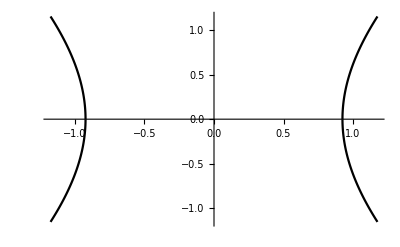

```mathematica
ListLinePlot[{PPHPBoundary,NPHPBoundary,NNHPBoundary,PNHPBoundary},PlotStyle->Black]
```

### Upper Cut Curve (LoC) in 2D

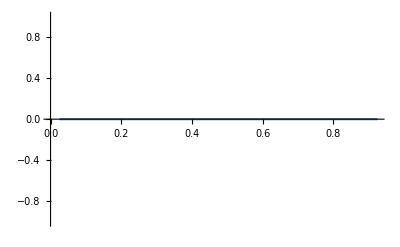

```mathematica
ListLinePlot[HPCutCurvein2D[{0.9250829011201859,0},{1193},{0,901,1}]]
```

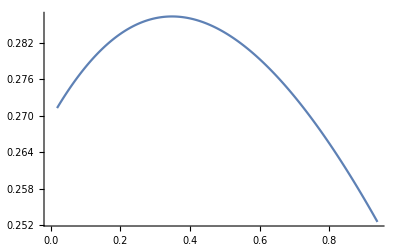

```mathematica
ListLinePlot[HPCutCurvein2D[{0.9250829011201859,0},{1193},{180,922,1}]]
```

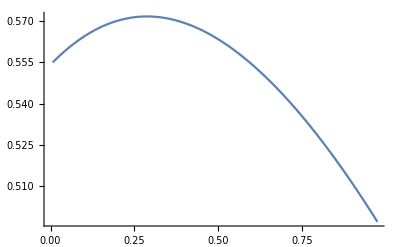

```mathematica
ListLinePlot[HPCutCurvein2D[{0.9250829011201859,0},{1193},{360,975,1}]]
```

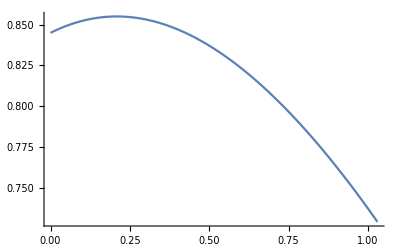

```mathematica
ListLinePlot[HPCutCurvein2D[{0.9250829011201859,0},{1193},{540,1043,1}]]
```

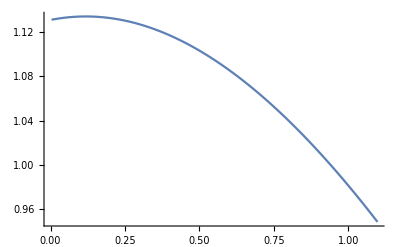

```mathematica
ListLinePlot[HPCutCurvein2D[{0.9250829011201859,0},{1193},{720,1118,1}]]
```

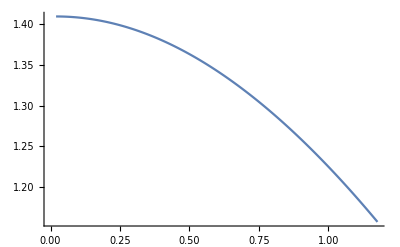

```mathematica
ListLinePlot[HPCutCurvein2D[{0.9250829011201859,0},{1193},{900,1193,1}]]
```

```mathematica
PPHPUpperCut0=HPCutCurvein2D[{0.9250829011201859,0},{1193},{0,901,1}][[870;;901]];
NPHPUpperCut0=Table[{-1,1},{i,1,32}]*PPHPUpperCut0;
NNHPUpperCut0=Table[{-1,-1},{i,1,32}]*PPHPUpperCut0;
PNHPUpperCut0=Table[{1,-1},{i,1,32}]*PPHPUpperCut0;
```

```mathematica
PPHPUpperCut180=HPCutCurvein2D[{0.9250829011201859,0},{1193},{180,922,1}];
NPHPUpperCut180=Table[{-1,1},{i,1,922}]*PPHPUpperCut180;
NNHPUpperCut180=Table[{-1,-1},{i,1,922}]*PPHPUpperCut180;
PNHPUpperCut180=Table[{1,-1},{i,1,922}]*PPHPUpperCut180;
```

```mathematica
PPHPUpperCut360=HPCutCurvein2D[{0.9250829011201859,0},{1193},{360,975,1}];
NPHPUpperCut360=Table[{-1,1},{i,1,975}]*PPHPUpperCut360;
NNHPUpperCut360=Table[{-1,-1},{i,1,975}]*PPHPUpperCut360;
PNHPUpperCut360=Table[{1,-1},{i,1,975}]*PPHPUpperCut360;
```

```mathematica
PPHPUpperCut540=HPCutCurvein2D[{0.9250829011201859,0},{1193},{540,1043,1}];
NPHPUpperCut540=Table[{-1,1},{i,1,1043}]*PPHPUpperCut540;
NNHPUpperCut540=Table[{-1,-1},{i,1,1043}]*PPHPUpperCut540;
PNHPUpperCut540=Table[{1,-1},{i,1,1043}]*PPHPUpperCut540;
```

```mathematica
PPHPUpperCut720=HPCutCurvein2D[{0.9250829011201859,0},{1193},{720,1118,1}];
NPHPUpperCut720=Table[{-1,1},{i,1,1118}]*PPHPUpperCut720;
NNHPUpperCut720=Table[{-1,-1},{i,1,1118}]*PPHPUpperCut720;
PNHPUpperCut720=Table[{1,-1},{i,1,1118}]*PPHPUpperCut720;
```

```mathematica
PPHPUpperCut900=HPCutCurvein2D[{0.9250829011201859,0},{1193},{900,1193,1}];
NPHPUpperCut900=Table[{-1,1},{i,1,1193}]*PPHPUpperCut900;
NNHPUpperCut900=Table[{-1,-1},{i,1,1193}]*PPHPUpperCut900;
PNHPUpperCut900=Table[{1,-1},{i,1,1193}]*PPHPUpperCut900;
```

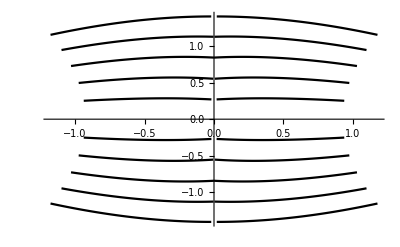

```mathematica
ListLinePlot[{
PPHPUpperCut180,NPHPUpperCut180,NNHPUpperCut180,PNHPUpperCut180,
PPHPUpperCut360,NPHPUpperCut360,NNHPUpperCut360,PNHPUpperCut360,
PPHPUpperCut540,NPHPUpperCut540,NNHPUpperCut540,PNHPUpperCut540,
PPHPUpperCut720,NPHPUpperCut720,NNHPUpperCut720,PNHPUpperCut720,
PPHPUpperCut900,NPHPUpperCut900,NNHPUpperCut900,PNHPUpperCut900},PlotStyle->Black]
```

### Lower Cut LoC in 2D

```mathematica
PPHPLowerCut0=HPEndPointin2D[{0.9250829011201859,0},{0,901},{180,922},{0,901},1];
NPHPLowerCut0=Table[{-1,1},{i,1,901}]*PPHPLowerCut0;
NNHPLowerCut0=Table[{-1,-1},{i,1,901}]*PPHPLowerCut0;
PNHPLowerCut0=Table[{1,-1},{i,1,901}]*PPHPLowerCut0;
```

```mathematica
PPHPLowerCut180=HPEndPointin2D[{0.9250829011201859,0},{180,922},{360,975},{0,901},1];
NPHPLowerCut180=Table[{-1,1},{i,1,901}]*PPHPLowerCut180;
NNHPLowerCut180=Table[{-1,-1},{i,1,901}]*PPHPLowerCut180;
PNHPLowerCut180=Table[{1,-1},{i,1,901}]*PPHPLowerCut180;
```

```mathematica
PPHPLowerCut360=HPEndPointin2D[{0.9250829011201859,0},{360,975},{540,1043},{0,901},1];
NPHPLowerCut360=Table[{-1,1},{i,1,901}]*PPHPLowerCut360;
NNHPLowerCut360=Table[{-1,-1},{i,1,901}]*PPHPLowerCut360;
PNHPLowerCut360=Table[{1,-1},{i,1,901}]*PPHPLowerCut360;
```

```mathematica
PPHPLowerCut540=HPEndPointin2D[{0.9250829011201859,0},{540,1043},{720,1118},{0,901},1];
NPHPLowerCut540=Table[{-1,1},{i,1,901}]*PPHPLowerCut540;
NNHPLowerCut540=Table[{-1,-1},{i,1,901}]*PPHPLowerCut540;
PNHPLowerCut540=Table[{1,-1},{i,1,901}]*PPHPLowerCut540;
```

```mathematica
PPHPLowerCut720=HPEndPointin2D[{0.9250829011201859,0},{720,1118},{900,1193},{0,901},1];
NPHPLowerCut720=Table[{-1,1},{i,1,901}]*PPHPLowerCut720;
NNHPLowerCut720=Table[{-1,-1},{i,1,901}]*PPHPLowerCut720;
PNHPLowerCut720=Table[{1,-1},{i,1,901}]*PPHPLowerCut720;
```

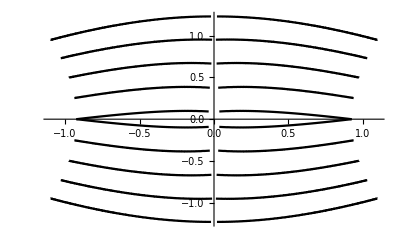

```mathematica
ListLinePlot[{PPHPLowerCut0,NPHPLowerCut0,NNHPLowerCut0,PNHPLowerCut0,
PPHPLowerCut180,NPHPLowerCut180,NNHPLowerCut180,PNHPLowerCut180,
PPHPLowerCut360,NPHPLowerCut360,NNHPLowerCut360,PNHPLowerCut360,
PPHPLowerCut540,NPHPLowerCut540,NNHPLowerCut540,PNHPLowerCut540,
PPHPLowerCut720,NPHPLowerCut720,NNHPLowerCut720,PNHPLowerCut720},PlotStyle->Black]
```

### Last Boundary in 2D

```mathematica
PPHPLastBoundary180=HPLastBoundary2D[{0.9250829011201859,0},{0,901},{180,922},{181},1];
NPHPLastBoundary180=Table[{-1,1},{i,1,181}]*PPHPLastBoundary180;
NNHPLastBoundary180=Table[{-1,-1},{i,1,181}]*PPHPLastBoundary180;
PNHPLastBoundary180=Table[{1,-1},{i,1,181}]*PPHPLastBoundary180;
```

```mathematica
PPHPLastBoundary360=HPLastBoundary2D[{0.9250829011201859,0},{180,922},{360,975},{181},1];
NPHPLastBoundary360=Table[{-1,1},{i,1,181}]*PPHPLastBoundary360;
NNHPLastBoundary360=Table[{-1,-1},{i,1,181}]*PPHPLastBoundary360;
PNHPLastBoundary360=Table[{1,-1},{i,1,181}]*PPHPLastBoundary360;
```

```mathematica
PPHPLastBoundary540=HPLastBoundary2D[{0.9250829011201859,0},{360,975},{540,1043},{181},1];
NPHPLastBoundary540=Table[{-1,1},{i,1,181}]*PPHPLastBoundary540;
NNHPLastBoundary540=Table[{-1,-1},{i,1,181}]*PPHPLastBoundary540;
PNHPLastBoundary540=Table[{1,-1},{i,1,181}]*PPHPLastBoundary540;
```

```mathematica
PPHPLastBoundary720=HPLastBoundary2D[{0.9250829011201859,0},{540,1043},{720,1118},{181},1];
NPHPLastBoundary720=Table[{-1,1},{i,1,181}]*PPHPLastBoundary720;
NNHPLastBoundary720=Table[{-1,-1},{i,1,181}]*PPHPLastBoundary720;
PNHPLastBoundary720=Table[{1,-1},{i,1,181}]*PPHPLastBoundary720;
```

```mathematica
PPHPLastBoundary900=HPLastBoundary2D[{0.9250829011201859,0},{720,1118},{900,1193},{181},1];
NPHPLastBoundary900=Table[{-1,1},{i,1,181}]*PPHPLastBoundary900;
NNHPLastBoundary900=Table[{-1,-1},{i,1,181}]*PPHPLastBoundary900;
PNHPLastBoundary900=Table[{1,-1},{i,1,181}]*PPHPLastBoundary900;
```

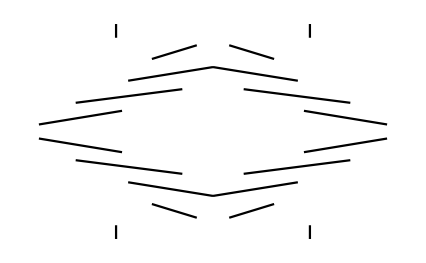

```mathematica
ListLinePlot[{PPHPLastBoundary180,NPHPLastBoundary180,NNHPLastBoundary180,PNHPLastBoundary180,
PPHPLastBoundary360,NPHPLastBoundary360,NNHPLastBoundary360,PNHPLastBoundary360,
PPHPLastBoundary540,NPHPLastBoundary540,NNHPLastBoundary540,PNHPLastBoundary540,
PPHPLastBoundary720,NPHPLastBoundary720,NNHPLastBoundary720,PNHPLastBoundary720,
PPHPLastBoundary900,NPHPLastBoundary900,NNHPLastBoundary900,PNHPLastBoundary900},PlotStyle->Black,Axes-> None]
```

## (a)

### Final in 2D

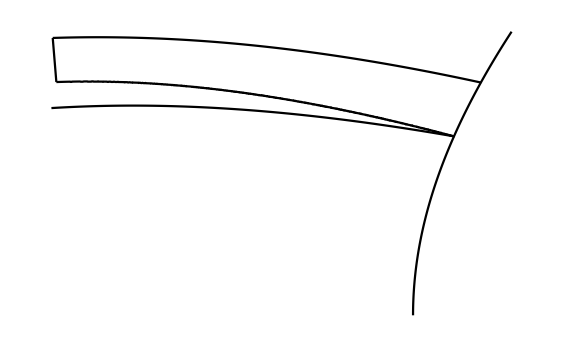

```mathematica
ListLinePlot[{PPHPBoundary,PPHPUpperCut540,PPHPUpperCut720,PPHPLowerCut540,PPHPLastBoundary720},PlotStyle->Black,PlotRange->All,Axes-> None]
```

(b)

## Set up

```mathematica
kernelcodeCPLAS2="
#define min 0
#define max 1
#define vvv 0
#define uuu 1
#define sign1 -1
#define h 0.001
#define n 1201
#define AlphaLAC (2.0)
#define BetaLASC (2.0)
#define InitRCLAC (1.0)
#define OmegaLASC (1.0)
#define Lambda_Max_LAC (12.718433357775211)
#define ArcLength_Max_LAC (6.764357890136049)
#define Lambda_Min_LAC (12.718433357775211)
#define ArcLength_Min_LAC (6.764357890136049)
#define Lambda_Max_LASC (6.285247558593747)
#define InitRT_Max_LASC (7.303131835937503)
#define ArcLength_Max_LASC (3.1084204465150833)
#define Lambda_Min_LASC (6.285247558593747)
#define InitRT_Min_LASC (7.303131835937503)
#define ArcLength_Min_LASC (3.1084204465150833)
#define Point00x (0.0)
#define Point00y (0.0)
#define Point00z (0.0)
#define Point03x (-0.7077264466498845)
#define Point03y (0.0)
#define Point03z (0.5008767232876717)
#define Point30x (0.0)
#define Point30y (-0.7077264466498845)
#define Point30z (-0.5008767232876717)
#define Point33x (-1.0013149889663)
#define Point33y (-1.0013149889663)
#define Point33z (0.0)

#define maxPoint00x (0.0)
#define maxPoint00y (0.0)
#define maxPoint00z (0.0)
#define maxPoint03x (-0.7077264357685561)
#define maxPoint03y (0.0)
#define maxPoint03z (0.5008767386038725)
#define maxPoint30x (0.0)
#define maxPoint30y (-0.7077264466498845)
#define maxPoint30z (-0.5008767232876717)
#define maxPoint33x (-1.0013149894892335)
#define maxPoint33y (-1.0013149882505217)
#define maxPoint33z (-0.0000000012420347421705752)


#define ScaleToOrigin_Max_LAC (0.13192213273168868)
#define ScaleToOrigin_Min_LAC (0.13192213273168868)
#define ScaleToOrigin_Max_LASC (0.38164258171833326)
#define ScaleToOrigin_Min_LASC (0.38164258171833326)

#define inidxdu1 ((1-pv)*(maxPoint00x-maxPoint03x)+pv*(maxPoint30x-maxPoint33x)-v1_x1+v2_x1+(1-pv)*u1_t1+pv*u2_t1)
#define inidxdu2 ((1-pv)*(maxPoint00y-maxPoint03y)+pv*(maxPoint30y-maxPoint33y)-v1_x2+v2_x2+(1-pv)*u1_t2+pv*u2_t2)
#define inidxdu3 ((1-pv)*(maxPoint00z-maxPoint03z)+pv*(maxPoint30z-maxPoint33z)-v1_x3+v2_x3+(1-pv)*u1_t3+pv*u2_t3)
#define inidxdv1 ((1-pu)*(maxPoint00x-maxPoint30x)+pu*(maxPoint03x-maxPoint33x)-u1_x1+u2_x1+(1-pu)*v1_t1+pu*v2_t1)
#define inidxdv2 ((1-pu)*(maxPoint00y-maxPoint30y)+pu*(maxPoint03y-maxPoint33y)-u1_x2+u2_x2+(1-pu)*v1_t2+pu*v2_t2)
#define inidxdv3 ((1-pu)*(maxPoint00z-maxPoint30z)+pu*(maxPoint03z-maxPoint33z)-u1_x3+u2_x3+(1-pu)*v1_t3+pu*v2_t3)

#define inid2xdu21 ((1-pv)*u1_dt1+pv*u2_dt1)
#define inid2xdu22 ((1-pv)*u1_dt2+pv*u2_dt2)
#define inid2xdu23 ((1-pv)*u1_dt3+pv*u2_dt3)
#define inid2xdv21 ((1-pu)*v1_dt1+pu*v2_dt1)
#define inid2xdv22 ((1-pu)*v1_dt2+pu*v2_dt2)
#define inid2xdv23 ((1-pu)*v1_dt3+pu*v2_dt3)
#define inid2xdudv1 (-maxPoint00x+maxPoint03x+maxPoint30x-maxPoint33x-u1_t1+u2_t1-v1_t1+v2_t1)
#define inid2xdudv2 (-maxPoint00y+maxPoint03y+maxPoint30y-maxPoint33y-u1_t2+u2_t2-v1_t2+v2_t2)
#define inid2xdudv3 (-maxPoint00z+maxPoint03z+maxPoint30z-maxPoint33z-u1_t3+u2_t3-v1_t3+v2_t3)

#define inid3xdu31 ((1-pv)*u1_d2t1+pv*u2_d2t1)
#define inid3xdu32 ((1-pv)*u1_d2t2+pv*u2_d2t2)
#define inid3xdu33 ((1-pv)*u1_d2t3+pv*u2_d2t3)
#define inid3xdv31 ((1-pu)*v1_d2t1+pu*v2_d2t1)
#define inid3xdv32 ((1-pu)*v1_d2t2+pu*v2_d2t2)
#define inid3xdv33 ((1-pu)*v1_d2t3+pu*v2_d2t3)
#define inid3xdu2dv1 (-u1_dt1+u2_dt1)
#define inid3xdu2dv2 (-u1_dt2+u2_dt2)
#define inid3xdu2dv3 (-u1_dt3+u2_dt3)
#define inid3xdudv21 (-v1_dt1+v2_dt1)
#define inid3xdudv22 (-v1_dt2+v2_dt2)
#define inid3xdudv23 (-v1_dt3+v2_dt3)

#define Coons_x1 ((1-pv)*u1_x1+pv*u2_x1+(1-pu)*v1_x1+pu*v2_x1-((1-pu)*(1-pv)*maxPoint00x+pu*(1-pv)*maxPoint03x+(1-pu)*pv*maxPoint30x+pu*pv*maxPoint33x))
#define Coons_x2 ((1-pv)*u1_x2+pv*u2_x2+(1-pu)*v1_x2+pu*v2_x2-((1-pu)*(1-pv)*maxPoint00y+pu*(1-pv)*maxPoint03y+(1-pu)*pv*maxPoint30y+pu*pv*maxPoint33y))
#define Coons_x3 ((1-pv)*u1_x3+pv*u2_x3+(1-pu)*v1_x3+pu*v2_x3-((1-pu)*(1-pv)*maxPoint00z+pu*(1-pv)*maxPoint03z+(1-pu)*pv*maxPoint30z+pu*pv*maxPoint33z))


#define repiniSurNorvec iniSurNorvec(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,normv_C)
#define repiniDSurNvDu iniDSurNvDu(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,dnormvdu_C)
#define repiniDSurNvDv iniDSurNvDv(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,dnormvdv_C)
#define repiniScalarSurNor iniScalarSurNor(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,Scal)
#define repinicoefE inicoefE(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repiniDEDu iniDEDu(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniDEDv iniDEDv(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repinicoefF inicoefF(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repiniDFDu iniDFDu(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniDFDv iniDFDv(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repinicoefG inicoefG(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repiniDGDu iniDGDu(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniDGDv iniDGDv(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repinicoefL inicoefL(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repinicoefM inicoefM(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repinicoefN inicoefN(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniGaussCurva iniGaussCurva(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniMeanCurva iniMeanCurva(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniMaxPrinci iniMaxPrinci(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniMinPrinci iniMinPrinci(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniPrinci iniPrinci(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)

#define repiniDcoefL_2 iniDcoefL_2(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,CoeffL)
#define repiniDcoefM_2 iniDcoefM_2(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,CoeffM)
#define repiniDcoefN_2 iniDcoefN_2(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,CoeffN)
#define repiniDGaussCurva_2 iniDGaussCurva_2(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,GCurva)
#define repiniDMeanCurva_2 iniDMeanCurva_2(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,MCurva)
#define repiniDPrinci_2 iniDPrinci_2(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,optimum,PCurva)
#define repiniEta iniEta(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniMiu  iniMiu(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDuDs iniDuDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDvDs iniDvDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDEDs iniDEDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDFDs iniDFDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDGDs iniDGDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDLDs iniDLDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,optimum)
#define repiniDMDs iniDMDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,optimum)
#define repiniDNDs iniDNDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,optimum)
#define repiniDPrinciDs iniDPrinciDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,optimum)
#define repiniDvDt iniDvDt(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDuDt iniDuDt(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDSurDs iniDSurDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum,tangv)
#define repiniSurNor iniSurNor(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,Snor_C)
#define repiniBinormalSur iniBinormalSur(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum,binormv_C)
#define repiniAlp1 iniAlp1(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum,Alp1_C)
#define repiniBeta1 iniBeta1(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,optimum)


#define opt1 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float normv_C[])
#define opt2 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3)
#define opt3 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3)
#define opt4 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,mint optimum)
 #define opt5 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,mint optimum,float tangv_C[])
#define opt6 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,float dnormv_C[])
#define opt7 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,float Scal[])
#define opt8 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u1_d2t1,float u1_d2t2,float u1_d2t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float u2_d2t1,float u2_d2t2,float u2_d2t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v1_d2t1,float v1_d2t2,float v1_d2t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,float v2_d2t1,float v2_d2t2,float v2_d2t3,float coeff[])
#define opt9 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u1_d2t1,float u1_d2t2,float u1_d2t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float u2_d2t1,float u2_d2t2,float u2_d2t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v1_d2t1,float v1_d2t2,float v1_d2t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,float v2_d2t1,float v2_d2t2,float v2_d2t3,mint optimum,float coeff[])
#define opt10 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u1_d2t1,float u1_d2t2,float u1_d2t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float u2_d2t1,float u2_d2t2,float u2_d2t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v1_d2t1,float v1_d2t2,float v1_d2t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,float v2_d2t1,float v2_d2t2,float v2_d2t3,mint optimum)
#define opt11 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,mint optimum,float Alph_C[])
#define opt12 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float Snor_C[])
#define opt13 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,mint optimum,float binormv_C[])
#define opt14 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u1_d2t1,float u1_d2t2,float u1_d2t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float u2_d2t1,float u2_d2t2,float u2_d2t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v1_d2t1,float v1_d2t2,float v1_d2t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,float v2_d2t1,float v2_d2t2,float v2_d2t3,mint optimum,float x[])

__device__ float inicurvature_LAC(float t,float Alpha,float Lambda,float InitRC,float Total_s) 
{
if(Alpha==-1)
	{return ((float) 1)/InitRC-Lambda*t*Total_s;}
else if(Alpha==0) 
	{return ((float) 1)/exp(Lambda*t*Total_s+log(InitRC));} 
else if(Alpha==1)
	{return ((float) 1)/(InitRC+Lambda*t*Total_s);}
else if(Alpha==2)
	{return ((float) 1)/sqrt(pow(InitRC,2)+((float) 2)*Lambda*t*Total_s);}
else
	{return pow(pow(InitRC,Alpha)+Lambda*Alpha*t*Total_s,-((float) 1)/Alpha);}
}

__device__ float inidcLACdx(float t,float Alpha,float Lambda,float InitRC,float Total_s) 
{
if(Alpha==-1)
	{return -Total_s*Lambda;}
else if(Alpha==0) 
	{return -Total_s*(Lambda*exp(-Lambda*t*Total_s))/InitRC;} 
else if(Alpha==1)
	{return -Total_s*Lambda/pow(InitRC+Lambda*t*Total_s,2);}
else if(Alpha==2)
	{return -Total_s*Lambda/sqrt(pow(pow(InitRC,2)+((float) 2)*Lambda*t*Total_s,3));}
else
	{return -Total_s*Lambda*pow(pow(InitRC,Alpha)+Lambda*Alpha*t*Total_s,-((float) 1)-((float) 1)/Alpha);}
}
__device__ float inid2cLACdx2(float t,float Alpha,float Lambda,float InitRC,float Total_s) 
{
if(Alpha==-1)
	{return 0;}
else if(Alpha==0) 
	{return pow(Total_s,2)*(pow(Lambda,2)*exp(-Lambda*t*Total_s))/InitRC;} 
else if(Alpha==1)
	{return pow(Total_s,2)*((float) 2)*pow(Lambda,2)/pow(InitRC+Lambda*t*Total_s,3);}
else if(Alpha==2)
	{return pow(Total_s,2)*(((float) 3)*pow(Lambda,2))/sqrt(pow(pow(InitRC,2)+((float) 2)*Lambda*t*Total_s,5));}
else
	{return (((float) 1)+Alpha)*pow(Total_s,2)*pow(Lambda,2)*pow(pow(InitRC,Alpha)+Lambda*Alpha*t*Total_s,-((float) 2)-((float) 1)/Alpha);}
}

__device__ float iniTorsion_LASC(float t,float Beta,float Omega,float InitRT,float Total_s) 
{
if(Beta==-1)
	{return ((float) 1)/InitRT-Omega*t*Total_s;}
else if(Beta==0) 
	{return ((float) 1)/exp(Omega*t*Total_s+log(InitRT));} 
else if(Beta==1)
	{return ((float) 1)/(InitRT+Omega*t*Total_s);}
else if(Beta==2)
	{return ((float) 1)/sqrt(pow(InitRT,2)+((float) 2)*Omega*t*Total_s);}
else
	{return pow(pow(InitRT,Beta)+Omega*Beta*t*Total_s,-((float) 1)/Beta);}
}

__device__ float inidtLASCdx(float t,float Beta,float Omega,float InitRT,float Total_s) 
{
if(Beta==-1)
	{return -Total_s*Omega;}
else if(Beta==0) 
	{return -Total_s*(Omega*exp(-Omega*t*Total_s))/InitRT;} 
else if(Beta==1)
	{return -Total_s*Omega/pow(InitRT+Omega*t*Total_s,2);}
else if(Beta==2)
	{return -Total_s*Omega/sqrt(pow(pow(InitRT,2)+((float) 2)*Omega*t*Total_s,3));}
else
	{return -Total_s*Omega*pow(pow(InitRT,Beta)+Omega*Beta*t*Total_s,-((float) 1)-((float) 1)/Beta);}
}

__device__ float inid2tLASCdx2(float t,float Beta,float Omega,float InitRT,float Total_s) 
{
if(Beta==-1)
	{return 0;}
else if(Beta==0) 
	{return pow(Total_s,2)*(pow(Omega,2)*exp(-Omega*t*Total_s))/InitRT;} 
else if(Beta==1)
	{return pow(Total_s,2)*((float) 2)*pow(Omega,2)/pow(InitRT+Omega*t*Total_s,3);}
else if(Beta==2)
	{return pow(Total_s,2)*(((float) 3)*pow(Omega,2))/sqrt(pow(pow(InitRT,2)+((float) 2)*Omega*t*Total_s,5));}
else
	{return (((float) 1)+Beta)*pow(Total_s,2)*pow(Omega,2)*pow(pow(InitRT,Beta)+Omega*Beta*t*Total_s,-((float) 2)-((float) 1)/Beta);}
}

__device__ void iniSurNorvec opt1 
{
	normv_C[0] =inidxdu2*inidxdv3-inidxdu3*inidxdv2; 
	normv_C[1] =inidxdu3*inidxdv1-inidxdu1*inidxdv3;
	normv_C[2] =inidxdu1*inidxdv2-inidxdu2*inidxdv1; 
}
__device__ void iniDSurNvDu opt6
{
	dnormv_C[0] =(inid2xdu22*inidxdv3-inid2xdu23*inidxdv2)+(inidxdu2*inid2xdudv3-inidxdu3*inid2xdudv2); 
	dnormv_C[1] =(inid2xdu23*inidxdv1-inid2xdu21*inidxdv3)+(inidxdu3*inid2xdudv1-inidxdu1*inid2xdudv3);
	dnormv_C[2] =(inid2xdu21*inidxdv2-inid2xdu22*inidxdv1)+(inidxdu1*inid2xdudv2-inidxdu2*inid2xdudv1); 
}
__device__ void iniDSurNvDv opt6
{
	dnormv_C[0] =(inid2xdudv2*inidxdv3-inid2xdudv3*inidxdv2)+(inidxdu2*inid2xdv23-inidxdu3*inid2xdv22); 
	dnormv_C[1] =(inid2xdudv3*inidxdv1-inid2xdudv1*inidxdv3)+(inidxdu3*inid2xdv21-inidxdu1*inid2xdv23); 
	dnormv_C[2] =(inid2xdudv1*inidxdv2-inid2xdudv2*inidxdv1)+(inidxdu1*inid2xdv22-inidxdu2*inid2xdv21); 
}

__device__ void iniScalarSurNor opt7
{
float ScalSNor,DScalSNorDu,DScalSNorDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];

repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;


ScalSNor = sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
DScalSNorDu = (normv_C[0]*dnormvdu_C[0]+normv_C[1]*dnormvdu_C[1]+normv_C[2]*dnormvdu_C[2])/ScalSNor;
DScalSNorDv = (normv_C[0]*dnormvdv_C[0]+normv_C[1]*dnormvdv_C[1]+normv_C[2]*dnormvdv_C[2])/ScalSNor;


Scal[0] = ScalSNor;
Scal[1] = DScalSNorDu;
Scal[2] = DScalSNorDv;
}

__device__ float inicoefE opt2
{
	return inidxdu1*inidxdu1+inidxdu2*inidxdu2+inidxdu3*inidxdu3; 
}
__device__ float iniDEDu opt3
{
	return 2*(inidxdu1*inid2xdu21+inidxdu2*inid2xdu22+inidxdu3*inid2xdu23);
}
__device__ float iniDEDv opt3
{
	return 2*(inidxdu1*inid2xdudv1+inidxdu2*inid2xdudv2+inidxdu3*inid2xdudv3);
}

 
__device__ float inicoefF opt2
{ 
	return (inidxdu1*inidxdv1+inidxdu2*inidxdv2+inidxdu3*inidxdv3); 
}
__device__ float iniDFDu opt3
{ 
	return inidxdv1*inid2xdu21+inidxdv2*inid2xdu22+inidxdv3*inid2xdu23 + inidxdu1*inid2xdudv1+inidxdu2*inid2xdudv2+inidxdu3*inid2xdudv3;
}
__device__ float iniDFDv opt3
{ 
	return inidxdv1*inid2xdudv1+inidxdv2*inid2xdudv2+inidxdv3*inid2xdudv3 + inidxdu1*inid2xdv21+inidxdu2*inid2xdv22+inidxdu3*inid2xdv23;
}

__device__ float inicoefG opt2
{ 
	return inidxdv1*inidxdv1+inidxdv2*inidxdv2+inidxdv3*inidxdv3; 
}
__device__ float iniDGDu opt3
{ 
	return 2*(inidxdv1*inid2xdudv1+inidxdv2*inid2xdudv2+inidxdv3*inid2xdudv3);
}
__device__ float iniDGDv opt3
{ 
	return 2*(inidxdv1*inid2xdv21+inidxdv2*inid2xdv22+inidxdv3*inid2xdv23);
}

__device__ float inicoefL opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdu21+normv_C[1]*inid2xdu22+normv_C[2]*inid2xdu23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float inicoefM opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdudv1+normv_C[1]*inid2xdudv2+normv_C[2]*inid2xdudv3)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float inicoefN opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdv21+normv_C[1]*inid2xdv22+normv_C[2]*inid2xdv23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float iniGaussCurva opt3
{
	return (repinicoefL*repinicoefN-pow(repinicoefM,2))/(repinicoefE*repinicoefG-pow(repinicoefF,2)); 
}
__device__ float iniMeanCurva opt3
{
	return 0.5*(repinicoefE*repinicoefN+repinicoefG*repinicoefL-2*repinicoefF*repinicoefM)/(repinicoefE*repinicoefG-pow(repinicoefF,2));
}
__device__ float iniMaxPrinci opt3
{
	return repiniMeanCurva+sqrt(pow(repiniMeanCurva,2)-repiniGaussCurva); 
}

__device__ float iniMinPrinci opt3
{
	return repiniMeanCurva-sqrt(pow(repiniMeanCurva,2)-repiniGaussCurva); 
}
__device__ float iniPrinci opt4
{ 	
	if(optimum==max) 
	{return repiniMaxPrinci;} 
	else if(optimum==min)
	{return repiniMinPrinci;}
	else
	{return 0;}
}
__device__ void iniDcoefL_2 opt8
{

float CoeL,DCoeLDu,DCoeLDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];

repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;
repiniScalarSurNor;

CoeL = (normv_C[0]*inid2xdu21+normv_C[1]*inid2xdu22+normv_C[2]*inid2xdu23)/Scal[0];
DCoeLDu = ((dnormvdu_C[0]*inid2xdu21+dnormvdu_C[1]*inid2xdu22+dnormvdu_C[2]*inid2xdu23)+(normv_C[0]*inid3xdu31+normv_C[1]*inid3xdu32+normv_C[2]*inid3xdu33)-Scal[1]*CoeL)/Scal[0];
DCoeLDv = ((dnormvdv_C[0]*inid2xdu21+dnormvdv_C[1]*inid2xdu22+dnormvdv_C[2]*inid2xdu23)+(normv_C[0]*inid3xdu2dv1+normv_C[1]*inid3xdu2dv2+normv_C[2]*inid3xdu2dv3)-Scal[2]*CoeL)/Scal[0];

coeff[0] = CoeL;
coeff[1] = DCoeLDu;
coeff[2] = DCoeLDv;

}
__device__ void iniDcoefM_2 opt8
{
float CoeM,DCoeMDu,DCoeMDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];
repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;
repiniScalarSurNor;

CoeM = (normv_C[0]*inid2xdudv1+normv_C[1]*inid2xdudv2+normv_C[2]*inid2xdudv3)/Scal[0];
DCoeMDu = ((dnormvdu_C[0]*inid2xdudv1+dnormvdu_C[1]*inid2xdudv2+dnormvdu_C[2]*inid2xdudv3)+(normv_C[0]*inid3xdu2dv1+normv_C[1]*inid3xdu2dv2+normv_C[2]*inid3xdu2dv3)-Scal[1]*CoeM)/Scal[0];
DCoeMDv = ((dnormvdv_C[0]*inid2xdudv1+dnormvdv_C[1]*inid2xdudv2+dnormvdv_C[2]*inid2xdudv3)+(normv_C[0]*inid3xdudv21+normv_C[1]*inid3xdudv22+normv_C[2]*inid3xdudv23)-Scal[2]*CoeM)/Scal[0];


coeff[0] = CoeM;
coeff[1] = DCoeMDu;
coeff[2] = DCoeMDv;
}
__device__ void iniDcoefN_2 opt8
{
float CoeN,DCoeNDu,DCoeNDv;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float Scal[3];
repiniSurNorvec;
repiniDSurNvDu;
repiniDSurNvDv;
repiniScalarSurNor;

CoeN = (normv_C[0]*inid2xdv21+normv_C[1]*inid2xdv22+normv_C[2]*inid2xdv23)/Scal[0];
DCoeNDu = ((dnormvdu_C[0]*inid2xdv21+dnormvdu_C[1]*inid2xdv22+dnormvdu_C[2]*inid2xdv23)+(normv_C[0]*inid3xdudv21+normv_C[1]*inid3xdudv22+normv_C[2]*inid3xdudv23)-Scal[1]*CoeN)/Scal[0];
DCoeNDv = ((dnormvdv_C[0]*inid2xdv21+dnormvdv_C[1]*inid2xdv22+dnormvdv_C[2]*inid2xdv23)+(normv_C[0]*inid3xdv31+normv_C[1]*inid3xdv32+normv_C[2]*inid3xdv33)-Scal[2]*CoeN)/Scal[0];

coeff[0] = CoeN;
coeff[1] = DCoeNDu;
coeff[2] = DCoeNDv;

}
__device__ void iniDGaussCurva_2 opt8 
{
float GCurv,DGCurvDu,DGCurvDv;
float CoeffL[3];
float CoeffM[3];
float CoeffN[3];
repiniDcoefL_2;
repiniDcoefM_2;
repiniDcoefN_2;

GCurv= (CoeffL[0]*CoeffN[0]-pow(CoeffM[0],2))/(repinicoefE*repinicoefG-pow(repinicoefF,2));
DGCurvDu = ((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repinicoefG*repiniDEDu-2*repinicoefF*repiniDFDu+repinicoefE*repiniDGDu)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*CoeffL[1]-2*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));
DGCurvDv =((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repinicoefG*repiniDEDv-2*repinicoefF*repiniDFDv+repinicoefE*repiniDGDv)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*CoeffL[2]-2*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));


coeff[0] = GCurv;
coeff[1] = DGCurvDu;
coeff[2] = DGCurvDv;

}
__device__ void iniDMeanCurva_2 opt8
{
float MCurv,DMCurvDu,DMCurvDv;
float CoeffL[3];
float CoeffM[3];
float CoeffN[3];
repiniDcoefL_2;
repiniDcoefM_2;
repiniDcoefN_2;

MCurv = 0.5*(repinicoefE*CoeffN[0]+repinicoefG*CoeffL[0]-2*repinicoefF*CoeffM[0])/(repinicoefE*repinicoefG-pow(repinicoefF,2));
DMCurvDu = 0.5*(-(repinicoefG*CoeffL[0]-2*repinicoefF*CoeffM[0]+repinicoefE*CoeffN[0])*(repinicoefG*repiniDEDu-2*repinicoefF*repiniDFDu+repinicoefE*repiniDGDu)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*repiniDEDu-2*CoeffM[0]*repiniDFDu+CoeffL[0]*repiniDGDu+repinicoefG*CoeffL[1]-2*repinicoefF*CoeffM[1]+repinicoefE*CoeffN[1]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));
DMCurvDv = 0.5*(-(repinicoefG*CoeffL[0]-2*repinicoefF*CoeffM[0]+repinicoefE*CoeffN[0])*(repinicoefG*repiniDEDv-2*repinicoefF*repiniDFDv+repinicoefE*repiniDGDv)+(-pow(repinicoefF,2)+repinicoefE*repinicoefG)*(CoeffN[0]*repiniDEDv-2*CoeffM[0]*repiniDFDv+CoeffL[0]*repiniDGDv+repinicoefG*CoeffL[2]-2*repinicoefF*CoeffM[2]+repinicoefE*CoeffN[2]))/(pow(pow(repinicoefF,2)-repinicoefE*repinicoefG,2));



coeff[0] = MCurv;
coeff[1] = DMCurvDu;
coeff[2] = DMCurvDv;
}
__device__ void iniDPrinci_2 opt9
{
float Princip,DPrincipDu,DPrincipDv;
float GCurva[3];
float MCurva[3];
repiniDGaussCurva_2;
repiniDMeanCurva_2;

if(optimum==max) 
{Princip = MCurva[0]+sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]+(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]+(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));

}
else if(optimum==min)
{Princip = MCurva[0]-sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]-(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]-(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));

}
else
{Princip = 0;
DPrincipDu = 0;
DPrincipDv = 0;
}

coeff[0] = Princip;
coeff[1] = DPrincipDu;
coeff[2] = DPrincipDv;

}

__device__ float iniEta opt4
{
	return sign1/sqrt(repinicoefE*pow(repinicoefM-repiniPrinci*repinicoefF,2)-2*repinicoefF*(repinicoefM-repiniPrinci*repinicoefF)*(repinicoefL-repiniPrinci*repinicoefE)+repinicoefG*pow(repinicoefL-repiniPrinci*repinicoefE,2));
}
__device__ float iniMiu opt4
{
	return sign1/sqrt(repinicoefE*pow(repinicoefN-repiniPrinci*repinicoefG,2)-2*repinicoefF*(repinicoefM-repiniPrinci*repinicoefF)*(repinicoefN-repiniPrinci*repinicoefG)+repinicoefG*pow(repinicoefM-repiniPrinci*repinicoefF,2));
}
__device__ float iniDuDs opt4
{ 
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return repiniEta*(repinicoefM-repiniPrinci*repinicoefF);}
else
	{return repiniMiu*(repinicoefN-repiniPrinci*repinicoefG);}
}
__device__ float iniDvDs opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return -repiniEta*(repinicoefL-repiniPrinci*repinicoefE);}
else
	{return -repiniMiu*(repinicoefM-repiniPrinci*repinicoefF);}
}


__device__ float iniDEDs opt4
{
	return repiniDEDu*repiniDuDs+repiniDEDv*repiniDvDs;
}
__device__ float iniDFDs opt4
{
	return repiniDFDu*repiniDuDs+repiniDFDv*repiniDvDs;
}
__device__ float iniDGDs opt4
{
	return repiniDGDu*repiniDuDs+repiniDGDv*repiniDvDs;
}
__device__ float iniDLDs opt10
{
float CoeffL[3];
repiniDcoefL_2;

	return CoeffL[1]*repiniDuDs+CoeffL[2]*repiniDvDs;
}
__device__ float iniDMDs opt10
{
float CoeffM[3];
repiniDcoefM_2;

	return CoeffM[1]*repiniDuDs+CoeffM[2]*repiniDvDs;
}
__device__ float iniDNDs opt10
{
float CoeffN[3];
repiniDcoefN_2;

	return CoeffN[1]*repiniDuDs+CoeffN[2]*repiniDvDs;
}
__device__ float iniDPrinciDs opt10
{
float PCurva[3];
repiniDPrinci_2;

	return PCurva[1]*repiniDuDs+PCurva[2]*repiniDvDs;
}
__device__ float iniDuDt opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return (repinicoefM-repiniPrinci*repinicoefF);}
else
	{return (repinicoefN-repiniPrinci*repinicoefG);}
}
__device__ float iniDvDt opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return (repinicoefL-repiniPrinci*repinicoefE);}
else
	{return (repinicoefM-repiniPrinci*repinicoefF);}
}
__device__ void iniDSurDs opt5
{
	tangv_C[0] =inidxdu1*repiniDuDs+inidxdv1*repiniDvDs;
	tangv_C[1] =inidxdu2*repiniDuDs+inidxdv2*repiniDvDs;
	tangv_C[2] =inidxdu3*repiniDuDs+inidxdv3*repiniDvDs;
}

__device__ void iniAlp1 opt11
{
	Alph_C[0]=(inid2xdu21*pow(repiniDuDs,2)+2*inid2xdudv1*repiniDuDs*repiniDvDs+inid2xdv21*pow(repiniDvDs,2));
	Alph_C[1]=(inid2xdu22*pow(repiniDuDs,2)+2*inid2xdudv2*repiniDuDs*repiniDvDs+inid2xdv22*pow(repiniDvDs,2));
	Alph_C[2]=(inid2xdu23*pow(repiniDuDs,2)+2*inid2xdudv3*repiniDuDs*repiniDvDs+inid2xdv23*pow(repiniDvDs,2));
}
__device__ void iniSurNor opt12 
{
	float normv_C[3];
	repiniSurNorvec;
	Snor_C[0] =normv_C[0]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]); 
	Snor_C[1] =normv_C[1]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
	Snor_C[2] =normv_C[2]/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]); 
}

__device__ void iniBinormalSur opt13
{
	float Snor_C[3];
	float tangv[3];
	repiniSurNor;
	repiniDSurDs;

	binormv_C[0] =Snor_C[1]*tangv[2] -Snor_C[2]*tangv[1];
	binormv_C[1] =Snor_C[2]*tangv[0] -Snor_C[0]*tangv[2];
	binormv_C[2] =Snor_C[0]*tangv[1] -Snor_C[1]*tangv[0];
}
__device__ float iniBeta1 opt10
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return (-(repiniDLDs-repiniDPrinciDs*repinicoefE-repiniPrinci*repiniDEDs)*repiniDuDs-(repiniDMDs-repiniDPrinciDs*repinicoefF-repiniPrinci*repiniDFDs)*repiniDvDs);}
else
	{return (-(repiniDMDs-repiniDPrinciDs*repinicoefF-repiniPrinci*repiniDFDs)*repiniDuDs-(repiniDNDs-repiniDPrinciDs*repinicoefG-repiniPrinci*repiniDGDs)*repiniDvDs);}
}

__device__ void LUDecomposition3x3 opt14
{
	mint rc=3;
	float binormv_C[3];
	float Alp1_C[3];
	repiniBinormalSur;
	repiniAlp1;
	float matrixA[3][3]={
	{repinicoefE,repinicoefF,-(binormv_C[0]*inidxdu1+binormv_C[1]*inidxdu2+binormv_C[2]*inidxdu3)},
	{repinicoefF,repinicoefG,-(binormv_C[0]*inidxdv1+binormv_C[1]*inidxdv2+binormv_C[2]*inidxdv3)},
	{repiniDvDt,repiniDuDt,0}};

	float matrixB[3]={-(Alp1_C[0]*inidxdu1+Alp1_C[1]*inidxdu2+Alp1_C[2]*inidxdu3),-(Alp1_C[0]*inidxdv1+Alp1_C[1]*inidxdv2+Alp1_C[2]*inidxdv3),repiniBeta1};
	float Lower[3][3];
	float Upper[3][3];
	float y[3];
	float sum;
	for(mint ii=0; ii<rc; ii++)
			{
				for(mint jj=0; jj<rc; jj++)
				{
					sum = 0;
					if(ii==jj)
					{
					Lower[ii][jj]=1;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else if(ii < jj) 
					{
					Lower[ii][jj]=0;
					for (mint kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else 
					{
					Upper[ii][jj]=0;
					for (mint kk = 0; kk < jj; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Lower[ii][jj] =(matrixA[ii][jj] - sum)/Upper[jj][jj];
					}
				}
			}
	for (mint ii = 0; ii < rc; ii++)
	{
		sum = 0;
		for (mint jj = 0; jj < ii; jj++)
			{sum += Lower[ii][jj] * y[jj];}
		y[ii] = matrixB[ii] - sum;
	}
	for (mint ii = rc - 1; ii >= 0; ii--)
	{
		sum = 0;
		for (mint jj = ii + 1; jj < rc; jj++)
			{sum += Upper[ii][jj] * x[jj];}
		x[ii] = (y[ii] - sum)/Upper[ii][ii];
	}
}


__device__ void RK4_LAC( float x1, float t1, float n1, float Alpha, float InitRC, float Lambda, float ArcLength, float initp, float stepsize, float& increment_x1, float& increment_t1, float& increment_n1) 
  
{
float x_k1,x_k2,x_k3,x_k4;
float t_k1,t_k2,t_k3,t_k4;
float n_k1,n_k2,n_k3,n_k4;
float newx1,newt1,newn1;

x_k1=stepsize*t1;
t_k1=stepsize*ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
n_k1=stepsize*ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t1);

newx1=x1+0.5*x_k1;
newt1=t1+0.5*t_k1;
newn1=n1+0.5*n_k1;
x_k2=stepsize*newt1;
t_k2=stepsize*ArcLength*(inicurvature_LAC(initp+0.5*stepsize,Alpha,Lambda,InitRC,ArcLength)*newn1);
n_k2=stepsize*ArcLength*(-inicurvature_LAC(initp+0.5*stepsize,Alpha,Lambda,InitRC,ArcLength)*newt1);

newx1=x1+0.5*x_k2;
newt1=t1+0.5*t_k2;
newn1=n1+0.5*n_k2;
x_k3=stepsize*newt1;
t_k3=stepsize*ArcLength*(inicurvature_LAC(initp+0.5*stepsize,Alpha,Lambda,InitRC,ArcLength)*newn1);
n_k3=stepsize*ArcLength*(-inicurvature_LAC(initp+0.5*stepsize,Alpha,Lambda,InitRC,ArcLength)*newt1);

newx1=x1+x_k3;
newt1=t1+t_k3;
newn1=n1+n_k3;
x_k4=stepsize*newt1;
t_k4=stepsize*ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*newn1);
n_k4=stepsize*ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*newt1);


increment_x1=(1.0/6.0)*(x_k1+2*x_k2+2*x_k3+x_k4);
increment_t1=(1.0/6.0)*(t_k1+2*t_k2+2*t_k3+t_k4);
increment_n1=(1.0/6.0)*(n_k1+2*n_k2+2*n_k3+n_k4);

}
__device__ void RK4_LASC( float x1, float t1, float n1, float b1, float Alpha, float Beta, float InitRC, float Omega, float Lambda, float InitRT, float ArcLength, float initp, float stepsize, float& increment_x1, float& increment_t1, float& increment_n1, float& increment_b1) 
  
{
float x_k1,x_k2,x_k3,x_k4;
float t_k1,t_k2,t_k3,t_k4;
float n_k1,n_k2,n_k3,n_k4;
float b_k1,b_k2,b_k3,b_k4;
float newx1,newt1,newn1,newb1;

x_k1=stepsize*t1;
t_k1=stepsize*ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
n_k1=stepsize*ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t1+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*b1);
b_k1=stepsize*ArcLength*(-iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*n1);

newx1=x1+0.5*x_k1;
newt1=t1+0.5*t_k1;
newn1=n1+0.5*n_k1;
newb1=b1+0.5*b_k1;
x_k2=stepsize*newt1;
t_k2=stepsize*ArcLength*(inicurvature_LAC(initp+0.5*stepsize,Alpha,Lambda,InitRC,ArcLength)*newn1);
n_k2=stepsize*ArcLength*(-inicurvature_LAC(initp+0.5*stepsize,Alpha,Lambda,InitRC,ArcLength)*newt1+iniTorsion_LASC(initp+0.5*stepsize,Beta,Omega,InitRT,ArcLength)*newb1);
b_k2=stepsize*ArcLength*(-iniTorsion_LASC(initp+0.5*stepsize,Beta,Omega,InitRT,ArcLength)*newn1);

newx1=x1+0.5*x_k2;
newt1=t1+0.5*t_k2;
newn1=n1+0.5*n_k2;
newb1=b1+0.5*b_k2;
x_k3=stepsize*newt1;
t_k3=stepsize*ArcLength*(inicurvature_LAC(initp+0.5*stepsize,Alpha,Lambda,InitRC,ArcLength)*newn1);
n_k3=stepsize*ArcLength*(-inicurvature_LAC(initp+0.5*stepsize,Alpha,Lambda,InitRC,ArcLength)*newt1+iniTorsion_LASC(initp+0.5*stepsize,Beta,Omega,InitRT,ArcLength)*newb1);
b_k3=stepsize*ArcLength*(-iniTorsion_LASC(initp+0.5*stepsize,Beta,Omega,InitRT,ArcLength)*newn1);

newx1=x1+x_k3;
newt1=t1+t_k3;
newn1=n1+n_k3;
newb1=b1+b_k3;
x_k4=stepsize*newt1;
t_k4=stepsize*ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*newn1);
n_k4=stepsize*ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*newt1+iniTorsion_LASC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*newb1);
b_k4=stepsize*ArcLength*(-iniTorsion_LASC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*newn1);

increment_x1=(1.0/6.0)*(x_k1+2*x_k2+2*x_k3+x_k4);
increment_t1=(1.0/6.0)*(t_k1+2*t_k2+2*t_k3+t_k4);
increment_n1=(1.0/6.0)*(n_k1+2*n_k2+2*n_k3+n_k4);
increment_b1=(1.0/6.0)*(b_k1+2*b_k2+2*b_k3+b_k4);

}

__device__ void First_Derivatives( float& dt1, float& dt2, float& dt3, float n1, float n2, float n3, float initp, float Alpha, float InitRC, float Lambda, float ArcLength)
{
dt1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
}


__device__ void FS_2ndDerivatives_LAC( float& dt1, float& dt2, float& dt3, float& d2t1, float& d2t2, float& d2t3, float t1, float t2, float t3, float n1, float n2, float n3, float initp, float Alpha, float InitRC, float Lambda, float ArcLength)
{
float dn1, dn2, dn3;

dt1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
dn1=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t1);
dn2=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t2);
dn3=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t3);

d2t1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn1+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
d2t2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn2+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
d2t3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn3+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n3);

}

__device__ void FS_2ndDerivatives_LASC( float& dt1, float& dt2, float& dt3, float& d2t1, float& d2t2, float& d2t3, float t1, float t2, float t3, float n1, float n2, float n3, float b1, float b2, float b3, float initp, float Alpha, float Beta, float InitRC, float Omega, float Lambda, float InitRT, float ArcLength)
{
float dn1, dn2, dn3;

dt1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
dn1=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t1+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*b1);
dn2=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t2+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*b2);
dn3=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t3+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*b3);

d2t1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn1+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
d2t2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn2+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
d2t3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn3+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
}


__device__ void FS_Derivatives_LAC( float& dt1, float& dt2, float& dt3, float& d2t1, float& d2t2, float& d2t3, float& d3t1, float& d3t2, float& d3t3, float t1, float t2, float t3, float n1, float n2, float n3, float initp, float Alpha, float InitRC, float Lambda, float ArcLength)
{
float dn1, dn2, dn3, d2n1, d2n2, d2n3;

dt1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
dn1=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t1);
dn2=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t2);
dn3=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t3);

d2t1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn1+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
d2t2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn2+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
d2t3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn3+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
d2n1=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dt1-inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*t1);
d2n2=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dt2-inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*t2);
d2n3=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dt3-inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*t3);

d3t1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*d2n1+2.0*inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*dn1+inid2cLACdx2(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
d3t2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*d2n2+2.0*inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*dn2+inid2cLACdx2(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
d3t3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*d2n3+2.0*inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*dn3+inid2cLACdx2(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
}


__device__ void FS_Derivatives_LASC( float& dt1, float& dt2, float& dt3, float& d2t1, float& d2t2, float& d2t3, float& d3t1, float& d3t2, float& d3t3, float t1, float t2, float t3, float n1, float n2, float n3, float b1, float b2, float b3, float initp, float Alpha, float Beta, float InitRC, float Omega, float Lambda, float InitRT, float ArcLength)
{
float dn1, dn2, dn3, d2n1, d2n2, d2n3;
float db1, db2, db3;

dt1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
dn1=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t1+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*b1);
dn2=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t2+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*b2);
dn3=ArcLength*(-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*t3+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*b3);
db1=ArcLength*(-iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*n1);
db2=ArcLength*(-iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*n2);
db3=ArcLength*(-iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*n3);

d2t1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn1+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
d2t2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn2+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
d2t3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dn3+inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
d2n1=ArcLength*(-inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*t1-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dt1+inidtLASCdx(initp,Beta,Omega,InitRT,ArcLength)*b1+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*db1);
d2n2=ArcLength*(-inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*t2-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dt2+inidtLASCdx(initp,Beta,Omega,InitRT,ArcLength)*b2+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*db2);
d2n3=ArcLength*(-inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*t3-inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*dt3+inidtLASCdx(initp,Beta,Omega,InitRT,ArcLength)*b3+iniTorsion_LASC(initp,Beta,Omega,InitRT,ArcLength)*db3);

d3t1=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*d2n1+2.0*inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*dn1+inid2cLACdx2(initp,Alpha,Lambda,InitRC,ArcLength)*n1);
d3t2=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*d2n2+2.0*inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*dn2+inid2cLACdx2(initp,Alpha,Lambda,InitRC,ArcLength)*n2);
d3t3=ArcLength*(inicurvature_LAC(initp,Alpha,Lambda,InitRC,ArcLength)*d2n3+2.0*inidcLACdx(initp,Alpha,Lambda,InitRC,ArcLength)*dn3+inid2cLACdx2(initp,Alpha,Lambda,InitRC,ArcLength)*n3);
}

__device__ void FS_LAC( float& x1, float& x2, float& x3, float& t1, float& t2, float& t3, float& n1, float& n2, float& n3, float Alpha, float InitRC, float Lambda, float ArcLength, float initp, float stepsize)
{
float increment_x1,increment_t1,increment_n1;
float increment_x2,increment_t2,increment_n2;
float increment_x3,increment_t3,increment_n3;

RK4_LAC(x1,t1,n1,Alpha,InitRC,Lambda,ArcLength,initp,stepsize,increment_x1,increment_t1,increment_n1);
RK4_LAC(x2,t2,n2,Alpha,InitRC,Lambda,ArcLength,initp,stepsize,increment_x2,increment_t2,increment_n2);
RK4_LAC(x3,t3,n3,Alpha,InitRC,Lambda,ArcLength,initp,stepsize,increment_x3,increment_t3,increment_n3);

x1+=increment_x1;
x2+=increment_x2;
x3+=increment_x3;
t1+=increment_t1;
t2+=increment_t2;
t3+=increment_t3;
n1+=increment_n1;
n2+=increment_n2;
n3+=increment_n3;
}

__device__ void FS_LASC( float& x1, float& x2, float& x3, float& t1, float& t2, float& t3, float& n1, float& n2, float& n3, float& b1, float& b2, float& b3, float Alpha, float Beta, float InitRC, float Omega, float Lambda, float InitRT, float ArcLength, float initp, float stepsize)
{
float increment_x1,increment_t1,increment_n1,increment_b1;
float increment_x2,increment_t2,increment_n2,increment_b2;
float increment_x3,increment_t3,increment_n3,increment_b3;

RK4_LASC(x1,t1,n1,b1,Alpha,Beta,InitRC,Omega,Lambda,InitRT,ArcLength,initp,stepsize,increment_x1,increment_t1,increment_n1,increment_b1);
RK4_LASC(x2,t2,n2,b2,Alpha,Beta,InitRC,Omega,Lambda,InitRT,ArcLength,initp,stepsize,increment_x2,increment_t2,increment_n2,increment_b2);
RK4_LASC(x3,t3,n3,b3,Alpha,Beta,InitRC,Omega,Lambda,InitRT,ArcLength,initp,stepsize,increment_x3,increment_t3,increment_n3,increment_b3);

x1+=increment_x1;
x2+=increment_x2;
x3+=increment_x3;
t1+=increment_t1;
t2+=increment_t2;
t3+=increment_t3;
n1+=increment_n1;
n2+=increment_n2;
n3+=increment_n3;
b1+=increment_b1;
b2+=increment_b2;
b3+=increment_b3;
}

__device__ void RK4_func_LoC( float pu, float pv, float u1_x1, float u1_x2, float u1_x3, float u1_t1, float u1_t2, float u1_t3, float u1_n1, float u1_n2, float u1_n3, float u2_x1, float u2_x2, float u2_x3, float u2_t1, float u2_t2, float u2_t3, float u2_n1, float u2_n2, float u2_n3, float u2_b1, float u2_b2, float u2_b3, float v1_x1, float v1_x2, float v1_x3, float v1_t1, float v1_t2, float v1_t3, float v1_n1, float v1_n2, float v1_n3, float v2_x1, float v2_x2, float v2_x3, float v2_t1, float v2_t2, float v2_t3, float v2_n1, float v2_n2, float v2_n3, float v2_b1, float v2_b2, float v2_b3, mint optimum, float stepsize, float& increment_u, float& increment_v)  
{
float u1_dt1, u1_dt2, u1_dt3, u2_dt1, u2_dt2, u2_dt3, v1_dt1, v1_dt2, v1_dt3, v2_dt1, v2_dt2, v2_dt3;
float pu_k1,pu_k2,pu_k3,pu_k4;
float pv_k1,pv_k2,pv_k3,pv_k4;
float increment_u1_x1, increment_u1_x2, increment_u1_x3, increment_u1_t1, increment_u1_t2, increment_u1_t3, increment_u1_n1, increment_u1_n2, increment_u1_n3;
float increment_u2_x1, increment_u2_x2, increment_u2_x3, increment_u2_t1, increment_u2_t2, increment_u2_t3, increment_u2_n1, increment_u2_n2, increment_u2_n3, increment_u2_b1, increment_u2_b2, increment_u2_b3;
float increment_v1_x1, increment_v1_x2, increment_v1_x3, increment_v1_t1, increment_v1_t2, increment_v1_t3, increment_v1_n1, increment_v1_n2, increment_v1_n3;
float increment_v2_x1, increment_v2_x2, increment_v2_x3, increment_v2_t1, increment_v2_t2, increment_v2_t3, increment_v2_n1, increment_v2_n2, increment_v2_n3, increment_v2_b1, increment_v2_b2, increment_v2_b3;
float new_pu, new_pv;
float new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u1_n1,new_u1_n2,new_u1_n3;
float new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_u2_n1,new_u2_n2,new_u2_n3;
float new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v1_n1,new_v1_n2,new_v1_n3;
float new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,new_v2_n1,new_v2_n2,new_v2_n3;


First_Derivatives(u1_dt1,u1_dt2,u1_dt3,u1_n1,u1_n2,u1_n3,pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
First_Derivatives(u2_dt1,u2_dt2,u2_dt3,u2_n1,u2_n2,u2_n3,pu,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC);
First_Derivatives(v1_dt1,v1_dt2,v1_dt3,v1_n1,v1_n2,v1_n3,pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
First_Derivatives(v2_dt1,v2_dt2,v2_dt3,v2_n1,v2_n2,v2_n3,pv,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC);

pu_k1=stepsize*iniDuDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);
pv_k1=stepsize*iniDvDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);

RK4_LAC(u1_x1,u1_t1,u1_n1,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k1,increment_u1_x1,increment_u1_t1,increment_u1_n1);
RK4_LAC(u1_x2,u1_t2,u1_n2,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k1,increment_u1_x2,increment_u1_t2,increment_u1_n2);
RK4_LAC(u1_x3,u1_t3,u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k1,increment_u1_x3,increment_u1_t3,increment_u1_n3);
RK4_LASC(u2_x1,u2_t1,u2_n1,u2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k1,increment_u2_x1,increment_u2_t1,increment_u2_n1,increment_u2_b1);
RK4_LASC(u2_x2,u2_t2,u2_n2,u2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k1,increment_u2_x2,increment_u2_t2,increment_u2_n2,increment_u2_b2);
RK4_LASC(u2_x3,u2_t3,u2_n3,u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k1,increment_u2_x3,increment_u2_t3,increment_u2_n3,increment_u2_b3);
RK4_LAC(v1_x1,v1_t1,v1_n1,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k1,increment_v1_x1,increment_v1_t1,increment_v1_n1);
RK4_LAC(v1_x2,v1_t2,v1_n2,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k1,increment_v1_x2,increment_v1_t2,increment_v1_n2);
RK4_LAC(v1_x3,v1_t3,v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k1,increment_v1_x3,increment_v1_t3,increment_v1_n3);
RK4_LASC(v2_x1,v2_t1,v2_n1,v2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k1,increment_v2_x1,increment_v2_t1,increment_v2_n1,increment_v2_b1);
RK4_LASC(v2_x2,v2_t2,v2_n2,v2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k1,increment_v2_x2,increment_v2_t2,increment_v2_n2,increment_v2_b2);
RK4_LASC(v2_x3,v2_t3,v2_n3,v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k1,increment_v2_x3,increment_v2_t3,increment_v2_n3,increment_v2_b3);

new_pu=pu+0.5*pu_k1;
new_pv=pv+0.5*pv_k1;
new_u1_x1=u1_x1+increment_u1_x1;
new_u1_x2=u1_x2+increment_u1_x2;
new_u1_x3=u1_x3+increment_u1_x3;
new_u1_t1=u1_t1+increment_u1_t1;
new_u1_t2=u1_t2+increment_u1_t2;
new_u1_t3=u1_t3+increment_u1_t3;
new_u1_n1=u1_n1+increment_u1_n1;
new_u1_n2=u1_n2+increment_u1_n2;
new_u1_n3=u1_n3+increment_u1_n3;
new_u2_x1=u2_x1+increment_u2_x1;
new_u2_x2=u2_x2+increment_u2_x2;
new_u2_x3=u2_x3+increment_u2_x3;
new_u2_t1=u2_t1+increment_u2_t1;
new_u2_t2=u2_t2+increment_u2_t2;
new_u2_t3=u2_t3+increment_u2_t3;
new_u2_n1=u2_n1+increment_u2_n1;
new_u2_n2=u2_n2+increment_u2_n2;
new_u2_n3=u2_n3+increment_u2_n3;
new_v1_x1=v1_x1+increment_v1_x1;
new_v1_x2=v1_x2+increment_v1_x2;
new_v1_x3=v1_x3+increment_v1_x3;
new_v1_t1=v1_t1+increment_v1_t1;
new_v1_t2=v1_t2+increment_v1_t2;
new_v1_t3=v1_t3+increment_v1_t3;
new_v1_n1=v1_n1+increment_v1_n1;
new_v1_n2=v1_n2+increment_v1_n2;
new_v1_n3=v1_n3+increment_v1_n3;
new_v2_x1=v2_x1+increment_v2_x1;
new_v2_x2=v2_x2+increment_v2_x2;
new_v2_x3=v2_x3+increment_v2_x3;
new_v2_t1=v2_t1+increment_v2_t1;
new_v2_t2=v2_t2+increment_v2_t2;
new_v2_t3=v2_t3+increment_v2_t3;
new_v2_n1=v2_n1+increment_v2_n1;
new_v2_n2=v2_n2+increment_v2_n2;
new_v2_n3=v2_n3+increment_v2_n3;

First_Derivatives(new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u1_n1,new_u1_n2,new_u1_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
First_Derivatives(new_u2_dt1,new_u2_dt2,new_u2_dt3,new_u2_n1,new_u2_n2,new_u2_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC);
First_Derivatives(new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v1_n1,new_v1_n2,new_v1_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
First_Derivatives(new_v2_dt1,new_v2_dt2,new_v2_dt3,new_v2_n1,new_v2_n2,new_v2_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC);


pu_k2=stepsize*iniDuDs(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);
pv_k2=stepsize*iniDvDs(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);

RK4_LAC(u1_x1,u1_t1,u1_n1,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k2,increment_u1_x1,increment_u1_t1,increment_u1_n1);
RK4_LAC(u1_x2,u1_t2,u1_n2,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k2,increment_u1_x2,increment_u1_t2,increment_u1_n2);
RK4_LAC(u1_x3,u1_t3,u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k2,increment_u1_x3,increment_u1_t3,increment_u1_n3);
RK4_LASC(u2_x1,u2_t1,u2_n1,u2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k2,increment_u2_x1,increment_u2_t1,increment_u2_n1,increment_u2_b1);
RK4_LASC(u2_x2,u2_t2,u2_n2,u2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k2,increment_u2_x2,increment_u2_t2,increment_u2_n2,increment_u2_b2);
RK4_LASC(u2_x3,u2_t3,u2_n3,u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k2,increment_u2_x3,increment_u2_t3,increment_u2_n3,increment_u2_b3);
RK4_LAC(v1_x1,v1_t1,v1_n1,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k2,increment_v1_x1,increment_v1_t1,increment_v1_n1);
RK4_LAC(v1_x2,v1_t2,v1_n2,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k2,increment_v1_x2,increment_v1_t2,increment_v1_n2);
RK4_LAC(v1_x3,v1_t3,v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k2,increment_v1_x3,increment_v1_t3,increment_v1_n3);
RK4_LASC(v2_x1,v2_t1,v2_n1,v2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k2,increment_v2_x1,increment_v2_t1,increment_v2_n1,increment_v2_b1);
RK4_LASC(v2_x2,v2_t2,v2_n2,v2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k2,increment_v2_x2,increment_v2_t2,increment_v2_n2,increment_v2_b2);
RK4_LASC(v2_x3,v2_t3,v2_n3,v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k2,increment_v2_x3,increment_v2_t3,increment_v2_n3,increment_v2_b3);

new_pu=pu+0.5*pu_k2;
new_pv=pv+0.5*pv_k2;
new_u1_x1=u1_x1+increment_u1_x1;
new_u1_x2=u1_x2+increment_u1_x2;
new_u1_x3=u1_x3+increment_u1_x3;
new_u1_t1=u1_t1+increment_u1_t1;
new_u1_t2=u1_t2+increment_u1_t2;
new_u1_t3=u1_t3+increment_u1_t3;
new_u1_n1=u1_n1+increment_u1_n1;
new_u1_n2=u1_n2+increment_u1_n2;
new_u1_n3=u1_n3+increment_u1_n3;
new_u2_x1=u2_x1+increment_u2_x1;
new_u2_x2=u2_x2+increment_u2_x2;
new_u2_x3=u2_x3+increment_u2_x3;
new_u2_t1=u2_t1+increment_u2_t1;
new_u2_t2=u2_t2+increment_u2_t2;
new_u2_t3=u2_t3+increment_u2_t3;
new_u2_n1=u2_n1+increment_u2_n1;
new_u2_n2=u2_n2+increment_u2_n2;
new_u2_n3=u2_n3+increment_u2_n3;
new_v1_x1=v1_x1+increment_v1_x1;
new_v1_x2=v1_x2+increment_v1_x2;
new_v1_x3=v1_x3+increment_v1_x3;
new_v1_t1=v1_t1+increment_v1_t1;
new_v1_t2=v1_t2+increment_v1_t2;
new_v1_t3=v1_t3+increment_v1_t3;
new_v1_n1=v1_n1+increment_v1_n1;
new_v1_n2=v1_n2+increment_v1_n2;
new_v1_n3=v1_n3+increment_v1_n3;
new_v2_x1=v2_x1+increment_v2_x1;
new_v2_x2=v2_x2+increment_v2_x2;
new_v2_x3=v2_x3+increment_v2_x3;
new_v2_t1=v2_t1+increment_v2_t1;
new_v2_t2=v2_t2+increment_v2_t2;
new_v2_t3=v2_t3+increment_v2_t3;
new_v2_n1=v2_n1+increment_v2_n1;
new_v2_n2=v2_n2+increment_v2_n2;
new_v2_n3=v2_n3+increment_v2_n3;

First_Derivatives(new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u1_n1,new_u1_n2,new_u1_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
First_Derivatives(new_u2_dt1,new_u2_dt2,new_u2_dt3,new_u2_n1,new_u2_n2,new_u2_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC);
First_Derivatives(new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v1_n1,new_v1_n2,new_v1_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
First_Derivatives(new_v2_dt1,new_v2_dt2,new_v2_dt3,new_v2_n1,new_v2_n2,new_v2_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC);


pu_k3=stepsize*iniDuDs(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);
pv_k3=stepsize*iniDvDs(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);

RK4_LAC(u1_x1,u1_t1,u1_n1,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,pu_k3,increment_u1_x1,increment_u1_t1,increment_u1_n1);
RK4_LAC(u1_x2,u1_t2,u1_n2,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,pu_k3,increment_u1_x2,increment_u1_t2,increment_u1_n2);
RK4_LAC(u1_x3,u1_t3,u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,pu_k3,increment_u1_x3,increment_u1_t3,increment_u1_n3);
RK4_LASC(u2_x1,u2_t1,u2_n1,u2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,pu_k3,increment_u2_x1,increment_u2_t1,increment_u2_n1,increment_u2_b1);
RK4_LASC(u2_x2,u2_t2,u2_n2,u2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,pu_k3,increment_u2_x2,increment_u2_t2,increment_u2_n2,increment_u2_b2);
RK4_LASC(u2_x3,u2_t3,u2_n3,u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,pu_k3,increment_u2_x3,increment_u2_t3,increment_u2_n3,increment_u2_b3);
RK4_LAC(v1_x1,v1_t1,v1_n1,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,pv_k3,increment_v1_x1,increment_v1_t1,increment_v1_n1);
RK4_LAC(v1_x2,v1_t2,v1_n2,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,pv_k3,increment_v1_x2,increment_v1_t2,increment_v1_n2);
RK4_LAC(v1_x3,v1_t3,v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,pv_k3,increment_v1_x3,increment_v1_t3,increment_v1_n3);
RK4_LASC(v2_x1,v2_t1,v2_n1,v2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,pv_k3,increment_v2_x1,increment_v2_t1,increment_v2_n1,increment_v2_b1);
RK4_LASC(v2_x2,v2_t2,v2_n2,v2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,pv_k3,increment_v2_x2,increment_v2_t2,increment_v2_n2,increment_v2_b2);
RK4_LASC(v2_x3,v2_t3,v2_n3,v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,pv_k3,increment_v2_x3,increment_v2_t3,increment_v2_n3,increment_v2_b3);

new_pu=pu+pu_k3;
new_pv=pv+pv_k3;
new_u1_x1=u1_x1+increment_u1_x1;
new_u1_x2=u1_x2+increment_u1_x2;
new_u1_x3=u1_x3+increment_u1_x3;
new_u1_t1=u1_t1+increment_u1_t1;
new_u1_t2=u1_t2+increment_u1_t2;
new_u1_t3=u1_t3+increment_u1_t3;
new_u1_n1=u1_n1+increment_u1_n1;
new_u1_n2=u1_n2+increment_u1_n2;
new_u1_n3=u1_n3+increment_u1_n3;
new_u2_x1=u2_x1+increment_u2_x1;
new_u2_x2=u2_x2+increment_u2_x2;
new_u2_x3=u2_x3+increment_u2_x3;
new_u2_t1=u2_t1+increment_u2_t1;
new_u2_t2=u2_t2+increment_u2_t2;
new_u2_t3=u2_t3+increment_u2_t3;
new_u2_n1=u2_n1+increment_u2_n1;
new_u2_n2=u2_n2+increment_u2_n2;
new_u2_n3=u2_n3+increment_u2_n3;
new_v1_x1=v1_x1+increment_v1_x1;
new_v1_x2=v1_x2+increment_v1_x2;
new_v1_x3=v1_x3+increment_v1_x3;
new_v1_t1=v1_t1+increment_v1_t1;
new_v1_t2=v1_t2+increment_v1_t2;
new_v1_t3=v1_t3+increment_v1_t3;
new_v1_n1=v1_n1+increment_v1_n1;
new_v1_n2=v1_n2+increment_v1_n2;
new_v1_n3=v1_n3+increment_v1_n3;
new_v2_x1=v2_x1+increment_v2_x1;
new_v2_x2=v2_x2+increment_v2_x2;
new_v2_x3=v2_x3+increment_v2_x3;
new_v2_t1=v2_t1+increment_v2_t1;
new_v2_t2=v2_t2+increment_v2_t2;
new_v2_t3=v2_t3+increment_v2_t3;
new_v2_n1=v2_n1+increment_v2_n1;
new_v2_n2=v2_n2+increment_v2_n2;
new_v2_n3=v2_n3+increment_v2_n3;

First_Derivatives(new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u1_n1,new_u1_n2,new_u1_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
First_Derivatives(new_u2_dt1,new_u2_dt2,new_u2_dt3,new_u2_n1,new_u2_n2,new_u2_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC);
First_Derivatives(new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v1_n1,new_v1_n2,new_v1_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
First_Derivatives(new_v2_dt1,new_v2_dt2,new_v2_dt3,new_v2_n1,new_v2_n2,new_v2_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC);


pu_k4=stepsize*iniDuDs(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);
pv_k4=stepsize*iniDvDs(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);

increment_u=(1.0/6.0)*(pu_k1+2*pu_k2+2*pu_k3+pu_k4);
increment_v=(1.0/6.0)*(pv_k1+2*pv_k2+2*pv_k3+pv_k4);

}


__device__ void ReturnDetail( mint k, float x[], float y[], float z[], float GeoCur[], mint optimum)
{
float u1_x1=Point00x, u1_x2=Point00y, u1_x3=Point00z;
float u2_x1=Point30x, u2_x2=Point30y, u2_x3=Point30z;
float v1_x1=Point00x, v1_x2=Point00y, v1_x3=Point00z;
float v2_x1=Point03x, v2_x2=Point03y, v2_x3=Point03z;

float u1_t1=-1*ScaleToOrigin_Max_LAC*ArcLength_Max_LAC, u1_t2=0, u1_t3=0;
float u1_n1=0, u1_n2=0, u1_n3=1*ScaleToOrigin_Max_LAC*ArcLength_Max_LAC;
float v1_t1=0, v1_t2=-1*ScaleToOrigin_Min_LAC*ArcLength_Min_LAC, v1_t3=0;
float v1_n1=0, v1_n2=0, v1_n3=-1*ScaleToOrigin_Min_LAC*ArcLength_Min_LAC;

float u2_t1=-1*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, u2_t2=0, u2_t3=0;
float u2_n1=0, u2_n2=-0.5930588126117428*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, u2_n3=0.8051591425200051*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC;
float u2_b1=0, u2_b2=0.8051591425200051*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, u2_b3=0.5930588126117428*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC;

float v2_t1=0, v2_t2=-1*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, v2_t3=0;
float v2_n1=-0.5930588126117428*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, v2_n2=0, v2_n3=-0.8051591425200051*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC;
float v2_b1=0.8051591425200051*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, v2_b2=0, v2_b3=-0.5930588126117428*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC;

float pu=0.0, pv=0.0;
float SSize_u, SSize_v, ratio;

float u1_dt1, u1_dt2, u1_dt3;
float u1_d2t1, u1_d2t2, u1_d2t3;
float u1_d3t1, u1_d3t2, u1_d3t3;
float u2_dt1, u2_dt2, u2_dt3;
float u2_d2t1, u2_d2t2, u2_d2t3;
float u2_d3t1, u2_d3t2, u2_d3t3;

float v1_dt1, v1_dt2, v1_dt3;
float v1_d2t1, v1_d2t2, v1_d2t3;
float v1_d3t1, v1_d3t2, v1_d3t3;
float v2_dt1, v2_dt2, v2_dt3;
float v2_d2t1, v2_d2t2, v2_d2t3;
float v2_d3t1, v2_d3t2, v2_d3t3;
float coef[3];


if(optimum==min)
{
	for(mint i=1;i<k+1;i++)
	{
	FS_LAC(u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_n1,u1_n2,u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,h);
	//increase u by 0.001, then return the details
	FS_LASC(u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_n1,u2_n2,u2_n3,u2_b1,u2_b2,u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,h);
	//increase u by 0.001, then return the details
	
	pu+=h;
	}
}
else if(optimum==max) 
{
	for(mint i=1;i<k+1;i++)
	{
	FS_LAC(v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_n1,v1_n2,v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,h);
	//increase v by 0.001, then return the details
	FS_LASC(v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_n1,v2_n2,v2_n3,v2_b1,v2_b2,v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,h);
	//increase v by 0.001, then return the details

	pv+=h;
	}
}

FS_2ndDerivatives_LAC(u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_t1,u1_t2,u1_t3,u1_n1,u1_n2,u1_n3,pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
FS_2ndDerivatives_LASC(u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_t1,u2_t2,u2_t3,u2_n1,u2_n2,u2_n3,u2_b1,u2_b2,u2_b3,pu,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC);
FS_2ndDerivatives_LAC(v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_t1,v1_t2,v1_t3,v1_n1,v1_n2,v1_n3,pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
FS_2ndDerivatives_LASC(v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_t1,v2_t2,v2_t3,v2_n1,v2_n2,v2_n3,v2_b1,v2_b2,v2_b3,pv,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC);
LUDecomposition3x3(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,optimum,coef);


x[0]=((1-pv)*u1_x1+pv*u2_x1+(1-pu)*v1_x1+pu*v2_x1-((1-pu)*(1-pv)*maxPoint00x+pu*(1-pv)*maxPoint03x+(1-pu)*pv*maxPoint30x+pu*pv*maxPoint33x));
y[0]=((1-pv)*u1_x2+pv*u2_x2+(1-pu)*v1_x2+pu*v2_x2-((1-pu)*(1-pv)*maxPoint00y+pu*(1-pv)*maxPoint03y+(1-pu)*pv*maxPoint30y+pu*pv*maxPoint33y));
z[0]=((1-pv)*u1_x3+pv*u2_x3+(1-pu)*v1_x3+pu*v2_x3-((1-pu)*(1-pv)*maxPoint00z+pu*(1-pv)*maxPoint03z+(1-pu)*pv*maxPoint30z+pu*pv*maxPoint33z));
GeoCur[0]=coef[2];


for(mint j=1;j<n;j++)
{
	RK4_func_LoC(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_n1,u1_n2,u1_n3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_n1,u2_n2,u2_n3,u2_b1,u2_b2,u2_b3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_n1,v1_n2,v1_n3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_n1,v2_n2,v2_n3,v2_b1,v2_b2,v2_b3,optimum,h,SSize_u,SSize_v);
	//return increment of u and v from duds and dvds

	if((pu+SSize_u) > 1.0)
		{
		if(pu==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-pu)/SSize_u;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}

	if((pv+SSize_v) > 1.0)
		{
		if(pv==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-pv)/SSize_v;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}
		FS_LAC(u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_n1,u1_n2,u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,SSize_u);
	//based on the increment of u as stepsize of LAC, then return the details
	FS_LASC(u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_n1,u2_n2,u2_n3,u2_b1,u2_b2,u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,SSize_u);
	//based on the incremnt of u as stepsize of LASC, then return the details
	FS_LAC(v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_n1,v1_n2,v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,SSize_v);
	//based on the increment of v as stepsize of LAC, then return the details
	FS_LASC(v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_n1,v2_n2,v2_n3,v2_b1,v2_b2,v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,SSize_v);
	//based on the increment of v as stepsize of LASC, then return the details

	pu+=SSize_u;		
	pv+=SSize_v;

	FS_2ndDerivatives_LAC(u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_t1,u1_t2,u1_t3,u1_n1,u1_n2,u1_n3,pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
	FS_2ndDerivatives_LASC(u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_t1,u2_t2,u2_t3,u2_n1,u2_n2,u2_n3,u2_b1,u2_b2,u2_b3,pu,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC);
	FS_2ndDerivatives_LAC(v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_t1,v1_t2,v1_t3,v1_n1,v1_n2,v1_n3,pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
	FS_2ndDerivatives_LASC(v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_t1,v2_t2,v2_t3,v2_n1,v2_n2,v2_n3,v2_b1,v2_b2,v2_b3,pv,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC);
	LUDecomposition3x3(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,optimum,coef);


	x[j]=((1-pv)*u1_x1+pv*u2_x1+(1-pu)*v1_x1+pu*v2_x1-((1-pu)*(1-pv)*maxPoint00x+pu*(1-pv)*maxPoint03x+(1-pu)*pv*maxPoint30x+pu*pv*maxPoint33x));
	y[j]=((1-pv)*u1_x2+pv*u2_x2+(1-pu)*v1_x2+pu*v2_x2-((1-pu)*(1-pv)*maxPoint00y+pu*(1-pv)*maxPoint03y+(1-pu)*pv*maxPoint30y+pu*pv*maxPoint33y));
	z[j]=((1-pv)*u1_x3+pv*u2_x3+(1-pu)*v1_x3+pu*v2_x3-((1-pu)*(1-pv)*maxPoint00z+pu*(1-pv)*maxPoint03z+(1-pu)*pv*maxPoint30z+pu*pv*maxPoint33z));
	GeoCur[j]=coef[2];

}

}

__device__ void ReturnXYZCoordinate( mint k, float x[], float y[], float z[], mint optimum)
{
float u1_x1=Point00x, u1_x2=Point00y, u1_x3=Point00z;
float u2_x1=Point30x, u2_x2=Point30y, u2_x3=Point30z;
float v1_x1=Point00x, v1_x2=Point00y, v1_x3=Point00z;
float v2_x1=Point03x, v2_x2=Point03y, v2_x3=Point03z;

float u1_t1=-1*ScaleToOrigin_Max_LAC*ArcLength_Max_LAC, u1_t2=0, u1_t3=0;
float u1_n1=0, u1_n2=0, u1_n3=1*ScaleToOrigin_Max_LAC*ArcLength_Max_LAC;
float v1_t1=0, v1_t2=-1*ScaleToOrigin_Min_LAC*ArcLength_Min_LAC, v1_t3=0;
float v1_n1=0, v1_n2=0, v1_n3=-1*ScaleToOrigin_Min_LAC*ArcLength_Min_LAC;

float u2_t1=-1*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, u2_t2=0, u2_t3=0;
float u2_n1=0, u2_n2=-0.5930588126117428*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, u2_n3=0.8051591425200051*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC;
float u2_b1=0, u2_b2=0.8051591425200051*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, u2_b3=0.5930588126117428*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC;

float v2_t1=0, v2_t2=-1*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, v2_t3=0;
float v2_n1=-0.5930588126117428*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, v2_n2=0, v2_n3=-0.8051591425200051*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC;
float v2_b1=0.8051591425200051*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, v2_b2=0, v2_b3=-0.5930588126117428*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC;

float pu=0.0, pv=0.0;
float SSize_u, SSize_v, ratio;

if(optimum==min)
{
	for(mint i=1;i<k+1;i++)
	{
	FS_LAC(u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_n1,u1_n2,u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,h);
	//increase u by 0.001, then return the details
	FS_LASC(u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_n1,u2_n2,u2_n3,u2_b1,u2_b2,u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,h);
	//increase u by 0.001, then return the details
	
	pu+=h;
	}
}
else if(optimum==max) 
{
	for(mint i=1;i<k+1;i++)
	{
	FS_LAC(v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_n1,v1_n2,v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,h);
	//increase v by 0.001, then return the details
	FS_LASC(v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_n1,v2_n2,v2_n3,v2_b1,v2_b2,v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,h);
	//increase v by 0.001, then return the details

	pv+=h;
	}
}


x[0]=((1-pv)*u1_x1+pv*u2_x1+(1-pu)*v1_x1+pu*v2_x1-((1-pu)*(1-pv)*maxPoint00x+pu*(1-pv)*maxPoint03x+(1-pu)*pv*maxPoint30x+pu*pv*maxPoint33x));
y[0]=((1-pv)*u1_x2+pv*u2_x2+(1-pu)*v1_x2+pu*v2_x2-((1-pu)*(1-pv)*maxPoint00y+pu*(1-pv)*maxPoint03y+(1-pu)*pv*maxPoint30y+pu*pv*maxPoint33y));
z[0]=((1-pv)*u1_x3+pv*u2_x3+(1-pu)*v1_x3+pu*v2_x3-((1-pu)*(1-pv)*maxPoint00z+pu*(1-pv)*maxPoint03z+(1-pu)*pv*maxPoint30z+pu*pv*maxPoint33z));



for(mint j=1;j<n;j++)
{
	RK4_func_LoC(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_n1,u1_n2,u1_n3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_n1,u2_n2,u2_n3,u2_b1,u2_b2,u2_b3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_n1,v1_n2,v1_n3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_n1,v2_n2,v2_n3,v2_b1,v2_b2,v2_b3,optimum,h,SSize_u,SSize_v);
	//return increment of u and v from duds and dvds

	if((pu+SSize_u) > 1.0)
		{
		if(pu==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-pu)/SSize_u;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}

	if((pv+SSize_v) > 1.0)
		{
		if(pv==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-pv)/SSize_v;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}

	FS_LAC(u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_n1,u1_n2,u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,SSize_u);
	//based on the increment of u as stepsize of LAC, then return the details
	FS_LASC(u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_n1,u2_n2,u2_n3,u2_b1,u2_b2,u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,SSize_u);
	//based on the incremnt of u as stepsize of LASC, then return the details
	FS_LAC(v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_n1,v1_n2,v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,SSize_v);
	//based on the increment of v as stepsize of LAC, then return the details
	FS_LASC(v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_n1,v2_n2,v2_n3,v2_b1,v2_b2,v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,SSize_v);
	//based on the increment of v as stepsize of LASC, then return the details

	pu+=SSize_u;		
	pv+=SSize_v;

	x[j]=((1-pv)*u1_x1+pv*u2_x1+(1-pu)*v1_x1+pu*v2_x1-((1-pu)*(1-pv)*maxPoint00x+pu*(1-pv)*maxPoint03x+(1-pu)*pv*maxPoint30x+pu*pv*maxPoint33x));
	y[j]=((1-pv)*u1_x2+pv*u2_x2+(1-pu)*v1_x2+pu*v2_x2-((1-pu)*(1-pv)*maxPoint00y+pu*(1-pv)*maxPoint03y+(1-pu)*pv*maxPoint30y+pu*pv*maxPoint33y));
	z[j]=((1-pv)*u1_x3+pv*u2_x3+(1-pu)*v1_x3+pu*v2_x3-((1-pu)*(1-pv)*maxPoint00z+pu*(1-pv)*maxPoint03z+(1-pu)*pv*maxPoint30z+pu*pv*maxPoint33z));
}

}


__device__ float DuDsforBoundaries opt4
{ 
if(optimum == max)
	{return 1.0/(sqrt(repinicoefE));}
else if(optimum == min)
	{return 0.0;}
}
__device__ float DvDsforBoundaries opt4
{
if(optimum == max)
	{return 0.0;}
else if(optimum == min)
	{return 1.0/(sqrt(repinicoefG));}
}

__device__ float GeoCurforBoundaries opt4
{ 
if(optimum == max)
	{return ((2.0*repinicoefE*repiniDFDu-repinicoefE*repiniDEDv-repinicoefF*repiniDEDu)*pow(DuDsforBoundaries(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum),3))/(2.0*sqrt(repinicoefE*repinicoefG-pow(repinicoefF,2)));}
else if(optimum == min)
	{return (-(2.0*repinicoefG*repiniDFDv-repinicoefG*repiniDGDu-repinicoefF*repiniDGDv)*pow(DvDsforBoundaries(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum),3))/(2.0*sqrt(repinicoefE*repinicoefG-pow(repinicoefF,2)));}
}

__device__ void RK4_func_Boundaries( float pu, float pv, float u1_x1, float u1_x2, float u1_x3, float u1_t1, float u1_t2, float u1_t3, float u1_n1, float u1_n2, float u1_n3, float u2_x1, float u2_x2, float u2_x3, float u2_t1, float u2_t2, float u2_t3, float u2_n1, float u2_n2, float u2_n3, float u2_b1, float u2_b2, float u2_b3, float v1_x1, float v1_x2, float v1_x3, float v1_t1, float v1_t2, float v1_t3, float v1_n1, float v1_n2, float v1_n3, float v2_x1, float v2_x2, float v2_x3, float v2_t1, float v2_t2, float v2_t3, float v2_n1, float v2_n2, float v2_n3, float v2_b1, float v2_b2, float v2_b3, mint optimum, float stepsize, float& increment_u, float& increment_v)  
{
float u1_dt1, u1_dt2, u1_dt3, u2_dt1, u2_dt2, u2_dt3, v1_dt1, v1_dt2, v1_dt3, v2_dt1, v2_dt2, v2_dt3;
float pu_k1,pu_k2,pu_k3,pu_k4;
float pv_k1,pv_k2,pv_k3,pv_k4;
float increment_u1_x1, increment_u1_x2, increment_u1_x3, increment_u1_t1, increment_u1_t2, increment_u1_t3, increment_u1_n1, increment_u1_n2, increment_u1_n3;
float increment_u2_x1, increment_u2_x2, increment_u2_x3, increment_u2_t1, increment_u2_t2, increment_u2_t3, increment_u2_n1, increment_u2_n2, increment_u2_n3, increment_u2_b1, increment_u2_b2, increment_u2_b3;
float increment_v1_x1, increment_v1_x2, increment_v1_x3, increment_v1_t1, increment_v1_t2, increment_v1_t3, increment_v1_n1, increment_v1_n2, increment_v1_n3;
float increment_v2_x1, increment_v2_x2, increment_v2_x3, increment_v2_t1, increment_v2_t2, increment_v2_t3, increment_v2_n1, increment_v2_n2, increment_v2_n3, increment_v2_b1, increment_v2_b2, increment_v2_b3;
float new_pu, new_pv;
float new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u1_n1,new_u1_n2,new_u1_n3;
float new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_u2_n1,new_u2_n2,new_u2_n3;
float new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v1_n1,new_v1_n2,new_v1_n3;
float new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,new_v2_n1,new_v2_n2,new_v2_n3;


First_Derivatives(u1_dt1,u1_dt2,u1_dt3,u1_n1,u1_n2,u1_n3,pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
First_Derivatives(u2_dt1,u2_dt2,u2_dt3,u2_n1,u2_n2,u2_n3,pu,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC);
First_Derivatives(v1_dt1,v1_dt2,v1_dt3,v1_n1,v1_n2,v1_n3,pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
First_Derivatives(v2_dt1,v2_dt2,v2_dt3,v2_n1,v2_n2,v2_n3,pv,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC);

pu_k1=stepsize*DuDsforBoundaries(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);
pv_k1=stepsize*DvDsforBoundaries(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);

RK4_LAC(u1_x1,u1_t1,u1_n1,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k1,increment_u1_x1,increment_u1_t1,increment_u1_n1);
RK4_LAC(u1_x2,u1_t2,u1_n2,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k1,increment_u1_x2,increment_u1_t2,increment_u1_n2);
RK4_LAC(u1_x3,u1_t3,u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k1,increment_u1_x3,increment_u1_t3,increment_u1_n3);
RK4_LASC(u2_x1,u2_t1,u2_n1,u2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k1,increment_u2_x1,increment_u2_t1,increment_u2_n1,increment_u2_b1);
RK4_LASC(u2_x2,u2_t2,u2_n2,u2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k1,increment_u2_x2,increment_u2_t2,increment_u2_n2,increment_u2_b2);
RK4_LASC(u2_x3,u2_t3,u2_n3,u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k1,increment_u2_x3,increment_u2_t3,increment_u2_n3,increment_u2_b3);
RK4_LAC(v1_x1,v1_t1,v1_n1,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k1,increment_v1_x1,increment_v1_t1,increment_v1_n1);
RK4_LAC(v1_x2,v1_t2,v1_n2,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k1,increment_v1_x2,increment_v1_t2,increment_v1_n2);
RK4_LAC(v1_x3,v1_t3,v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k1,increment_v1_x3,increment_v1_t3,increment_v1_n3);
RK4_LASC(v2_x1,v2_t1,v2_n1,v2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k1,increment_v2_x1,increment_v2_t1,increment_v2_n1,increment_v2_b1);
RK4_LASC(v2_x2,v2_t2,v2_n2,v2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k1,increment_v2_x2,increment_v2_t2,increment_v2_n2,increment_v2_b2);
RK4_LASC(v2_x3,v2_t3,v2_n3,v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k1,increment_v2_x3,increment_v2_t3,increment_v2_n3,increment_v2_b3);

new_pu=pu+0.5*pu_k1;
new_pv=pv+0.5*pv_k1;
new_u1_x1=u1_x1+increment_u1_x1;
new_u1_x2=u1_x2+increment_u1_x2;
new_u1_x3=u1_x3+increment_u1_x3;
new_u1_t1=u1_t1+increment_u1_t1;
new_u1_t2=u1_t2+increment_u1_t2;
new_u1_t3=u1_t3+increment_u1_t3;
new_u1_n1=u1_n1+increment_u1_n1;
new_u1_n2=u1_n2+increment_u1_n2;
new_u1_n3=u1_n3+increment_u1_n3;
new_u2_x1=u2_x1+increment_u2_x1;
new_u2_x2=u2_x2+increment_u2_x2;
new_u2_x3=u2_x3+increment_u2_x3;
new_u2_t1=u2_t1+increment_u2_t1;
new_u2_t2=u2_t2+increment_u2_t2;
new_u2_t3=u2_t3+increment_u2_t3;
new_u2_n1=u2_n1+increment_u2_n1;
new_u2_n2=u2_n2+increment_u2_n2;
new_u2_n3=u2_n3+increment_u2_n3;
new_v1_x1=v1_x1+increment_v1_x1;
new_v1_x2=v1_x2+increment_v1_x2;
new_v1_x3=v1_x3+increment_v1_x3;
new_v1_t1=v1_t1+increment_v1_t1;
new_v1_t2=v1_t2+increment_v1_t2;
new_v1_t3=v1_t3+increment_v1_t3;
new_v1_n1=v1_n1+increment_v1_n1;
new_v1_n2=v1_n2+increment_v1_n2;
new_v1_n3=v1_n3+increment_v1_n3;
new_v2_x1=v2_x1+increment_v2_x1;
new_v2_x2=v2_x2+increment_v2_x2;
new_v2_x3=v2_x3+increment_v2_x3;
new_v2_t1=v2_t1+increment_v2_t1;
new_v2_t2=v2_t2+increment_v2_t2;
new_v2_t3=v2_t3+increment_v2_t3;
new_v2_n1=v2_n1+increment_v2_n1;
new_v2_n2=v2_n2+increment_v2_n2;
new_v2_n3=v2_n3+increment_v2_n3;

First_Derivatives(new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u1_n1,new_u1_n2,new_u1_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
First_Derivatives(new_u2_dt1,new_u2_dt2,new_u2_dt3,new_u2_n1,new_u2_n2,new_u2_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC);
First_Derivatives(new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v1_n1,new_v1_n2,new_v1_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
First_Derivatives(new_v2_dt1,new_v2_dt2,new_v2_dt3,new_v2_n1,new_v2_n2,new_v2_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC);


pu_k2=stepsize*DuDsforBoundaries(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);
pv_k2=stepsize*DvDsforBoundaries(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);

RK4_LAC(u1_x1,u1_t1,u1_n1,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k2,increment_u1_x1,increment_u1_t1,increment_u1_n1);
RK4_LAC(u1_x2,u1_t2,u1_n2,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k2,increment_u1_x2,increment_u1_t2,increment_u1_n2);
RK4_LAC(u1_x3,u1_t3,u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,0.5*pu_k2,increment_u1_x3,increment_u1_t3,increment_u1_n3);
RK4_LASC(u2_x1,u2_t1,u2_n1,u2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k2,increment_u2_x1,increment_u2_t1,increment_u2_n1,increment_u2_b1);
RK4_LASC(u2_x2,u2_t2,u2_n2,u2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k2,increment_u2_x2,increment_u2_t2,increment_u2_n2,increment_u2_b2);
RK4_LASC(u2_x3,u2_t3,u2_n3,u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,0.5*pu_k2,increment_u2_x3,increment_u2_t3,increment_u2_n3,increment_u2_b3);
RK4_LAC(v1_x1,v1_t1,v1_n1,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k2,increment_v1_x1,increment_v1_t1,increment_v1_n1);
RK4_LAC(v1_x2,v1_t2,v1_n2,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k2,increment_v1_x2,increment_v1_t2,increment_v1_n2);
RK4_LAC(v1_x3,v1_t3,v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,0.5*pv_k2,increment_v1_x3,increment_v1_t3,increment_v1_n3);
RK4_LASC(v2_x1,v2_t1,v2_n1,v2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k2,increment_v2_x1,increment_v2_t1,increment_v2_n1,increment_v2_b1);
RK4_LASC(v2_x2,v2_t2,v2_n2,v2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k2,increment_v2_x2,increment_v2_t2,increment_v2_n2,increment_v2_b2);
RK4_LASC(v2_x3,v2_t3,v2_n3,v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,0.5*pv_k2,increment_v2_x3,increment_v2_t3,increment_v2_n3,increment_v2_b3);

new_pu=pu+0.5*pu_k2;
new_pv=pv+0.5*pv_k2;
new_u1_x1=u1_x1+increment_u1_x1;
new_u1_x2=u1_x2+increment_u1_x2;
new_u1_x3=u1_x3+increment_u1_x3;
new_u1_t1=u1_t1+increment_u1_t1;
new_u1_t2=u1_t2+increment_u1_t2;
new_u1_t3=u1_t3+increment_u1_t3;
new_u1_n1=u1_n1+increment_u1_n1;
new_u1_n2=u1_n2+increment_u1_n2;
new_u1_n3=u1_n3+increment_u1_n3;
new_u2_x1=u2_x1+increment_u2_x1;
new_u2_x2=u2_x2+increment_u2_x2;
new_u2_x3=u2_x3+increment_u2_x3;
new_u2_t1=u2_t1+increment_u2_t1;
new_u2_t2=u2_t2+increment_u2_t2;
new_u2_t3=u2_t3+increment_u2_t3;
new_u2_n1=u2_n1+increment_u2_n1;
new_u2_n2=u2_n2+increment_u2_n2;
new_u2_n3=u2_n3+increment_u2_n3;
new_v1_x1=v1_x1+increment_v1_x1;
new_v1_x2=v1_x2+increment_v1_x2;
new_v1_x3=v1_x3+increment_v1_x3;
new_v1_t1=v1_t1+increment_v1_t1;
new_v1_t2=v1_t2+increment_v1_t2;
new_v1_t3=v1_t3+increment_v1_t3;
new_v1_n1=v1_n1+increment_v1_n1;
new_v1_n2=v1_n2+increment_v1_n2;
new_v1_n3=v1_n3+increment_v1_n3;
new_v2_x1=v2_x1+increment_v2_x1;
new_v2_x2=v2_x2+increment_v2_x2;
new_v2_x3=v2_x3+increment_v2_x3;
new_v2_t1=v2_t1+increment_v2_t1;
new_v2_t2=v2_t2+increment_v2_t2;
new_v2_t3=v2_t3+increment_v2_t3;
new_v2_n1=v2_n1+increment_v2_n1;
new_v2_n2=v2_n2+increment_v2_n2;
new_v2_n3=v2_n3+increment_v2_n3;

First_Derivatives(new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u1_n1,new_u1_n2,new_u1_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
First_Derivatives(new_u2_dt1,new_u2_dt2,new_u2_dt3,new_u2_n1,new_u2_n2,new_u2_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC);
First_Derivatives(new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v1_n1,new_v1_n2,new_v1_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
First_Derivatives(new_v2_dt1,new_v2_dt2,new_v2_dt3,new_v2_n1,new_v2_n2,new_v2_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC);


pu_k3=stepsize*DuDsforBoundaries(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);
pv_k3=stepsize*DvDsforBoundaries(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);

RK4_LAC(u1_x1,u1_t1,u1_n1,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,pu_k3,increment_u1_x1,increment_u1_t1,increment_u1_n1);
RK4_LAC(u1_x2,u1_t2,u1_n2,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,pu_k3,increment_u1_x2,increment_u1_t2,increment_u1_n2);
RK4_LAC(u1_x3,u1_t3,u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,pu_k3,increment_u1_x3,increment_u1_t3,increment_u1_n3);
RK4_LASC(u2_x1,u2_t1,u2_n1,u2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,pu_k3,increment_u2_x1,increment_u2_t1,increment_u2_n1,increment_u2_b1);
RK4_LASC(u2_x2,u2_t2,u2_n2,u2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,pu_k3,increment_u2_x2,increment_u2_t2,increment_u2_n2,increment_u2_b2);
RK4_LASC(u2_x3,u2_t3,u2_n3,u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,pu_k3,increment_u2_x3,increment_u2_t3,increment_u2_n3,increment_u2_b3);
RK4_LAC(v1_x1,v1_t1,v1_n1,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,pv_k3,increment_v1_x1,increment_v1_t1,increment_v1_n1);
RK4_LAC(v1_x2,v1_t2,v1_n2,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,pv_k3,increment_v1_x2,increment_v1_t2,increment_v1_n2);
RK4_LAC(v1_x3,v1_t3,v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,pv_k3,increment_v1_x3,increment_v1_t3,increment_v1_n3);
RK4_LASC(v2_x1,v2_t1,v2_n1,v2_b1,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,pv_k3,increment_v2_x1,increment_v2_t1,increment_v2_n1,increment_v2_b1);
RK4_LASC(v2_x2,v2_t2,v2_n2,v2_b2,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,pv_k3,increment_v2_x2,increment_v2_t2,increment_v2_n2,increment_v2_b2);
RK4_LASC(v2_x3,v2_t3,v2_n3,v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,pv_k3,increment_v2_x3,increment_v2_t3,increment_v2_n3,increment_v2_b3);

new_pu=pu+pu_k3;
new_pv=pv+pv_k3;
new_u1_x1=u1_x1+increment_u1_x1;
new_u1_x2=u1_x2+increment_u1_x2;
new_u1_x3=u1_x3+increment_u1_x3;
new_u1_t1=u1_t1+increment_u1_t1;
new_u1_t2=u1_t2+increment_u1_t2;
new_u1_t3=u1_t3+increment_u1_t3;
new_u1_n1=u1_n1+increment_u1_n1;
new_u1_n2=u1_n2+increment_u1_n2;
new_u1_n3=u1_n3+increment_u1_n3;
new_u2_x1=u2_x1+increment_u2_x1;
new_u2_x2=u2_x2+increment_u2_x2;
new_u2_x3=u2_x3+increment_u2_x3;
new_u2_t1=u2_t1+increment_u2_t1;
new_u2_t2=u2_t2+increment_u2_t2;
new_u2_t3=u2_t3+increment_u2_t3;
new_u2_n1=u2_n1+increment_u2_n1;
new_u2_n2=u2_n2+increment_u2_n2;
new_u2_n3=u2_n3+increment_u2_n3;
new_v1_x1=v1_x1+increment_v1_x1;
new_v1_x2=v1_x2+increment_v1_x2;
new_v1_x3=v1_x3+increment_v1_x3;
new_v1_t1=v1_t1+increment_v1_t1;
new_v1_t2=v1_t2+increment_v1_t2;
new_v1_t3=v1_t3+increment_v1_t3;
new_v1_n1=v1_n1+increment_v1_n1;
new_v1_n2=v1_n2+increment_v1_n2;
new_v1_n3=v1_n3+increment_v1_n3;
new_v2_x1=v2_x1+increment_v2_x1;
new_v2_x2=v2_x2+increment_v2_x2;
new_v2_x3=v2_x3+increment_v2_x3;
new_v2_t1=v2_t1+increment_v2_t1;
new_v2_t2=v2_t2+increment_v2_t2;
new_v2_t3=v2_t3+increment_v2_t3;
new_v2_n1=v2_n1+increment_v2_n1;
new_v2_n2=v2_n2+increment_v2_n2;
new_v2_n3=v2_n3+increment_v2_n3;

First_Derivatives(new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u1_n1,new_u1_n2,new_u1_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
First_Derivatives(new_u2_dt1,new_u2_dt2,new_u2_dt3,new_u2_n1,new_u2_n2,new_u2_n3,new_pu,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC);
First_Derivatives(new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v1_n1,new_v1_n2,new_v1_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
First_Derivatives(new_v2_dt1,new_v2_dt2,new_v2_dt3,new_v2_n1,new_v2_n2,new_v2_n3,new_pv,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC);


pu_k4=stepsize*DuDsforBoundaries(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);
pv_k4=stepsize*DvDsforBoundaries(new_pu,new_pv,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);

increment_u=(1.0/6.0)*(pu_k1+2*pu_k2+2*pu_k3+pu_k4);
increment_v=(1.0/6.0)*(pv_k1+2*pv_k2+2*pv_k3+pv_k4);

}

__device__ void ReturnDetailforBoundaries( mint k, float x[], float y[], float z[], float GeoCur[], mint optimum)
{
float u1_x1=Point00x, u1_x2=Point00y, u1_x3=Point00z;
float u2_x1=Point30x, u2_x2=Point30y, u2_x3=Point30z;
float v1_x1=Point00x, v1_x2=Point00y, v1_x3=Point00z;
float v2_x1=Point03x, v2_x2=Point03y, v2_x3=Point03z;

float u1_t1=-1*ScaleToOrigin_Max_LAC*ArcLength_Max_LAC, u1_t2=0, u1_t3=0;
float u1_n1=0, u1_n2=0, u1_n3=1*ScaleToOrigin_Max_LAC*ArcLength_Max_LAC;
float v1_t1=0, v1_t2=-1*ScaleToOrigin_Min_LAC*ArcLength_Min_LAC, v1_t3=0;
float v1_n1=0, v1_n2=0, v1_n3=-1*ScaleToOrigin_Min_LAC*ArcLength_Min_LAC;

float u2_t1=-1*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, u2_t2=0, u2_t3=0;
float u2_n1=0, u2_n2=-0.5930588126117428*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, u2_n3=0.8051591425200051*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC;
float u2_b1=0, u2_b2=0.8051591425200051*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, u2_b3=0.5930588126117428*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC;

float v2_t1=0, v2_t2=-1*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, v2_t3=0;
float v2_n1=-0.5930588126117428*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, v2_n2=0, v2_n3=-0.8051591425200051*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC;
float v2_b1=0.8051591425200051*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, v2_b2=0, v2_b3=-0.5930588126117428*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC;

float u1_dt1,u1_dt2,u1_dt3;
float u2_dt1,u2_dt2,u2_dt3;
float v1_dt1,v1_dt2,v1_dt3;
float v2_dt1,v2_dt2,v2_dt3;

float pu=0.0, pv=0.0;
float SSize_u, SSize_v, ratio;


if(optimum==min)
{
	for(mint i=1;i<k+1;i++)
	{
	FS_LAC(u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_n1,u1_n2,u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,h);
	//increase u by 0.001, then return the details
	FS_LASC(u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_n1,u2_n2,u2_n3,u2_b1,u2_b2,u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,h);
	//increase u by 0.001, then return the details
	
	pu+=h;
	}
}
else if(optimum==max) 
{
	for(mint i=1;i<k+1;i++)
	{
	FS_LAC(v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_n1,v1_n2,v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,h);
	//increase v by 0.001, then return the details
	FS_LASC(v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_n1,v2_n2,v2_n3,v2_b1,v2_b2,v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,h);
	//increase v by 0.001, then return the details

	pv+=h;
	}
}
First_Derivatives(u1_dt1,u1_dt2,u1_dt3,u1_n1,u1_n2,u1_n3,pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
First_Derivatives(u2_dt1,u2_dt2,u2_dt3,u2_n1,u2_n2,u2_n3,pu,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC);
First_Derivatives(v1_dt1,v1_dt2,v1_dt3,v1_n1,v1_n2,v1_n3,pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
First_Derivatives(v2_dt1,v2_dt2,v2_dt3,v2_n1,v2_n2,v2_n3,pv,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC);


x[0]=((1-pv)*u1_x1+pv*u2_x1+(1-pu)*v1_x1+pu*v2_x1-((1-pu)*(1-pv)*maxPoint00x+pu*(1-pv)*maxPoint03x+(1-pu)*pv*maxPoint30x+pu*pv*maxPoint33x));
y[0]=((1-pv)*u1_x2+pv*u2_x2+(1-pu)*v1_x2+pu*v2_x2-((1-pu)*(1-pv)*maxPoint00y+pu*(1-pv)*maxPoint03y+(1-pu)*pv*maxPoint30y+pu*pv*maxPoint33y));
z[0]=((1-pv)*u1_x3+pv*u2_x3+(1-pu)*v1_x3+pu*v2_x3-((1-pu)*(1-pv)*maxPoint00z+pu*(1-pv)*maxPoint03z+(1-pu)*pv*maxPoint30z+pu*pv*maxPoint33z));
GeoCur[0]=GeoCurforBoundaries(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);

for(mint j=1;j<n;j++)
{
	RK4_func_Boundaries(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_n1,u1_n2,u1_n3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_n1,u2_n2,u2_n3,u2_b1,u2_b2,u2_b3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_n1,v1_n2,v1_n3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_n1,v2_n2,v2_n3,v2_b1,v2_b2,v2_b3,optimum,h,SSize_u,SSize_v);
	//return increment of u and v from duds and dvds

	if((pu+SSize_u) > 1.0)
		{
		if(pu==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-pu)/SSize_u;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}

	if((pv+SSize_v) > 1.0)
		{
		if(pv==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-pv)/SSize_v;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}
		FS_LAC(u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_n1,u1_n2,u1_n3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,pu,SSize_u);
	//based on the increment of u as stepsize of LAC, then return the details
	FS_LASC(u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_n1,u2_n2,u2_n3,u2_b1,u2_b2,u2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,pu,SSize_u);
	//based on the incremnt of u as stepsize of LASC, then return the details
	FS_LAC(v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_n1,v1_n2,v1_n3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,pv,SSize_v);
	//based on the increment of v as stepsize of LAC, then return the details
	FS_LASC(v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_n1,v2_n2,v2_n3,v2_b1,v2_b2,v2_b3,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,pv,SSize_v);
	//based on the increment of v as stepsize of LASC, then return the details

	pu+=SSize_u;		
	pv+=SSize_v;

	First_Derivatives(u1_dt1,u1_dt2,u1_dt3,u1_n1,u1_n2,u1_n3,pu,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);
	First_Derivatives(u2_dt1,u2_dt2,u2_dt3,u2_n1,u2_n2,u2_n3,pu,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC);
	First_Derivatives(v1_dt1,v1_dt2,v1_dt3,v1_n1,v1_n2,v1_n3,pv,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);
	First_Derivatives(v2_dt1,v2_dt2,v2_dt3,v2_n1,v2_n2,v2_n3,pv,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC);


	x[j]=((1-pv)*u1_x1+pv*u2_x1+(1-pu)*v1_x1+pu*v2_x1-((1-pu)*(1-pv)*maxPoint00x+pu*(1-pv)*maxPoint03x+(1-pu)*pv*maxPoint30x+pu*pv*maxPoint33x));
	y[j]=((1-pv)*u1_x2+pv*u2_x2+(1-pu)*v1_x2+pu*v2_x2-((1-pu)*(1-pv)*maxPoint00y+pu*(1-pv)*maxPoint03y+(1-pu)*pv*maxPoint30y+pu*pv*maxPoint33y));
	z[j]=((1-pv)*u1_x3+pv*u2_x3+(1-pu)*v1_x3+pu*v2_x3-((1-pu)*(1-pv)*maxPoint00z+pu*(1-pv)*maxPoint03z+(1-pu)*pv*maxPoint30z+pu*pv*maxPoint33z));
	GeoCur[j]=GeoCurforBoundaries(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);

}

}
__device__ float RK4_Init(float x1, float t1, float SSize) 
  
{
float k1,k2,k3,k4;

k1=SSize*x1;
k2=SSize*(x1+0.5*SSize*t1);
k3=SSize*(x1+0.5*SSize*t1);
k4=SSize*(x1+SSize*t1);

return (1.0/6.0)*(k1+2*k2+2*k3+k4);
}

__device__ void Init_Curve_2D_Boundaries( float GeoCur[],  float init_x, float init_y, float x[], float y[], float tangent1[], float tangent2[], float normal1[], float normal2[], mint optimum)
{//use to compute plane curve coordinates from given geodesic curvature
float DummyGeoCur1,DummyGeoCur2,DGCDs;
float x1, x2;
float t1, t2, dt1, dt2, d2t1, d2t2;
float n1, n2, dn1, dn2, d2n1, d2n2;

x1=init_x;
x2=init_y;

if (optimum==max)//when curve render in maximum principle direction, the tangent is {-1,0,0} at (-x)(-y) plane. We cross {-1,0,0}x{0,0,1} then we get normal is {0,1,0}. Then we flip the curve from (-x)(-y) plane to (-x)(y) plane we get tangent is {-1,0,0} and normal is {0,-1,0}. Finally we flip the curve from (-x)(y) plane to (x)(y) plane then we have tangent {1,0,0} and normal is {0,-1,0}.
{
	t1=1;
	t2=0;
	n1=0;
	n2=-1;
}
else if(optimum==min)//when curve render in minimum principle direction, the tangent is {0,-1,0} at (-x)(-y) plane. We cross {0,-1,0}x{0,0,1} then we get normal is {-1,0,0}. Then we flip the curve from (-x)(-y) plane to (-x)(y) plane we get tangent is {0,1,0} and normal is {-1,0,0}. Finally we flip the curve from (-x)(y) plane to (x)(y) plane then we have tangent {0,1,0} and normal is {1,0,0}.
{
	t1=0;
	t2=1;
	n1=1;
	n2=0;
}

x[0]=x1;
y[0]=x2;
tangent1[0]=t1;
tangent2[0]=t2;
normal1[0]=n1;
normal2[0]=n2;

for(mint j=1;j<n;j++)
{

DummyGeoCur1=GeoCur[j-1];
DummyGeoCur2=GeoCur[j];
DGCDs=(DummyGeoCur2-DummyGeoCur1)/h;
dt1=DummyGeoCur1*n1;
dt2=DummyGeoCur1*n2;
dn1=-DummyGeoCur1*t1;
dn2=-DummyGeoCur1*t2;
d2t1=DummyGeoCur1*dn1+DGCDs*n1;
d2t2=DummyGeoCur1*dn2+DGCDs*n2;
d2n1=-DummyGeoCur1*dt1-DGCDs*t1;
d2n2=-DummyGeoCur1*dt2-DGCDs*t2;

x1=x1+RK4_Init(t1,dt1,h);
x2=x2+RK4_Init(t2,dt2,h);
t1=t1+RK4_Init(dt1,d2t1,h);
t2=t2+RK4_Init(dt2,d2t2,h);
n1=n1+RK4_Init(dn1,d2n1,h);
n2=n2+RK4_Init(dn2,d2n2,h);

x[j]=x1;
y[j]=x2;
tangent1[j]=t1;
tangent2[j]=t2;
normal1[j]=n1;
normal2[j]=n2;
}

}


__device__ void CutCurve_2D( float GeoCur[], mint max_n, float init_x, float init_y, float init_t1, float init_t2, float init_n1, float init_n2, float x[], float y[], float tangent1[], float tangent2[], float normal1[], float normal2[], mint optimum)
{//use to compute plane curve coordinates from given geodesic curvature
float DummyGeoCur1,DummyGeoCur2,DGCDs;
float x1, x2;
float t1, t2, dt1, dt2, d2t1, d2t2;
float n1, n2, dn1, dn2, d2n1, d2n2;

x1=init_x;
x2=init_y;

if (optimum==max)//when curve render in maximum principle direction, the tangent is {-1,0,0} at (-x)(-y) plane. We cross {-1,0,0}x{0,0,1} then we get normal is {0,1,0}. Then we flip the curve from (-x)(-y) plane to (-x)(y) plane we get tangent is {-1,0,0} and normal is {0,-1,0}. Finally we flip the curve from (-x)(y) plane to (x)(y) plane then we have tangent {1,0,0} and normal is {0,-1,0}. Then we reverse the normal={0,1,0} so that we can cut out the pieces
{
	t1=-init_n1;
	t2=-init_n2;
	n1=init_t1;
	n2=init_t2;
}
else if(optimum==min)//when curve render in minimum principle direction, the tangent is {0,-1,0} at (-x)(-y) plane. We cross {0,-1,0}x{0,0,1} then we get normal is {-1,0,0}. Then we flip the curve from (-x)(-y) plane to (-x)(y) plane we get tangent is {0,1,0} and normal is {-1,0,0}. Finally we flip the curve from (-x)(y) plane to (x)(y) plane then we have tangent {0,1,0} and normal is {1,0,0}. Then we reverse the normal={-1,0,0} so that we can cut out the pieces
{
	t1=init_n1;
	t2=init_n2;
	n1=-init_t1;
	n2=-init_t2;
}

x[max_n]=x1;
y[max_n]=x2;
tangent1[max_n]=t1;
tangent2[max_n]=t2;
normal1[max_n]=n1;
normal2[max_n]=n2;

for(mint j=max_n-1;j>=0;j--)
{

DummyGeoCur1=GeoCur[j+1];
DummyGeoCur2=GeoCur[j];
DGCDs=(DummyGeoCur2-DummyGeoCur1)/h;
dt1=DummyGeoCur1*n1;
dt2=DummyGeoCur1*n2;
dn1=-DummyGeoCur1*t1;
dn2=-DummyGeoCur1*t2;
d2t1=DummyGeoCur1*dn1+DGCDs*n1;
d2t2=DummyGeoCur1*dn2+DGCDs*n2;
d2n1=-DummyGeoCur1*dt1-DGCDs*t1;
d2n2=-DummyGeoCur1*dt2-DGCDs*t2;

x1=x1+RK4_Init(t1,dt1,h);
x2=x2+RK4_Init(t2,dt2,h);
t1=t1+RK4_Init(dt1,d2t1,h);
t2=t2+RK4_Init(dt2,d2t2,h);
n1=n1+RK4_Init(dn1,d2n1,h);
n2=n2+RK4_Init(dn2,d2n2,h);


x[j]=x1;
y[j]=x2;
tangent1[j]=t1;
tangent2[j]=t2;
normal1[j]=n1;
normal2[j]=n2;
}

}

__device__ void ReturnInteger( mint& min_i, float x1[], float y1[], float z1[], float x2[], float y2[], float z2[])
{
float dif1;
float min_dif1=5;

for(mint i=0; i<n; i++)
{
	for(mint j=0; j<n; j++)
	{
		dif1=pow(x1[i]-x2[j],2)+pow(y1[i]-y2[j],2)+pow(z1[i]-z2[j],2);
		
		if (dif1<min_dif1)
		{
			min_dif1=dif1;
			min_i=i;
		}
	}
}
}

__device__ void ReturnPointsPosition( mint& res_i, mint& res_min_j, mint& res_max_j, float x1[], float y1[], float z1[], float x2[], float y2[], float z2[], float x3[], float y3[], float z3[])  
{
mint min_i;
mint min_j, max_j;
float dif1, dif2;
float min_dif1=5;
float min_dif2=5;

for(mint i=0; i<n; i++)
{
	for(mint j=0; j<n; j++)
	{
		dif1=pow(x1[i]-x3[j],2)+pow(y1[i]-y3[j],2)+pow(z1[i]-z3[j],2);
		dif2=pow(x2[i]-x3[j],2)+pow(y2[i]-y3[j],2)+pow(z2[i]-z3[j],2);
		
		if (dif1<min_dif1)
		{
			min_dif1=dif1;
			min_j=j;
		}

		if (dif2<min_dif2)
		{
			min_dif2=dif2;
			min_i=i;
			max_j=j;
		}
	}
}

res_i=min_i;
res_min_j=min_j;
res_max_j=max_j;

}


__device__ void ObtainSmallerPiece( mint res_i, mint min_j, mint max_j, float GeoCur[], float x_2d[], float y_2d[], float t1_2d[], float t2_2d[], float n1_2d[], float n2_2d[], float& resx, float& resy, mint optimum)  
{
float DummyGeoCur1,DummyGeoCur2,DGCDs;
float x1, x2;
float t1, t2, dt1, dt2, d2t1, d2t2;
float n1, n2, dn1, dn2, d2n1, d2n2;


x1=x_2d[res_i];
x2=y_2d[res_i];

if (optimum==max)//Since the 1st curve is in minimum principle direction (from curve to cut) and its tangent is tangent1={0,1} and normal is normal1={-1,0}. The orthogonal curve is rendered in maximum principle direction , hence tangent is tangento={1,0}=-normal1 and normal is normalo={0,-1}=-tangent1.
{
	t1=n1_2d[res_i];
	t2=n2_2d[res_i];
	n1=t1_2d[res_i];
	n2=t2_2d[res_i];

}
else if(optimum==min)//Since the 1st curve is in maximum principle direction (from curve to cut) and its tangent is tangent1={1,0} and normal is normal1={0,1}. The orthogonal curve is rendered in minimum principle direction , hence tangent is tangento={0,1}=normal1 and normal is normalo={1,0}=tangent1.
{
	t1=-n1_2d[res_i];
	t2=-n2_2d[res_i];
	n1=-t1_2d[res_i];
	n2=-t2_2d[res_i];
}

for(mint j=max_j-1;j>=min_j;j--)
{

DummyGeoCur1=GeoCur[j+1];
DummyGeoCur2=GeoCur[j];
DGCDs=(DummyGeoCur2-DummyGeoCur1)/h;
dt1=DummyGeoCur1*n1;
dt2=DummyGeoCur1*n2;
dn1=-DummyGeoCur1*t1;
dn2=-DummyGeoCur1*t2;
d2t1=DummyGeoCur1*dn1+DGCDs*n1;
d2t2=DummyGeoCur1*dn2+DGCDs*n2;
d2n1=-DummyGeoCur1*dt1-DGCDs*t1;
d2n2=-DummyGeoCur1*dt2-DGCDs*t2;

x1=x1+RK4_Init(t1,dt1,h);
x2=x2+RK4_Init(t2,dt2,h);
t1=t1+RK4_Init(dt1,d2t1,h);
t2=t2+RK4_Init(dt2,d2t2,h);
n1=n1+RK4_Init(dn1,d2n1,h);
n2=n2+RK4_Init(dn2,d2n2,h);
}

resx=x1;
resy=x2;

}

__device__ void SmallerPieceBoundary( float resx[], float resy[], float GeoCur[], mint min_j, mint max_j, float x_2d, float y_2d, float t1_2d, float t2_2d, float n1_2d, float n2_2d, mint optimum)  
{
float DummyGeoCur1,DummyGeoCur2,DGCDs;
float x1, x2;
float t1, t2, dt1, dt2, d2t1, d2t2;
float n1, n2, dn1, dn2, d2n1, d2n2;


x1=x_2d;
x2=y_2d;

if (optimum==max)//Since the 1st curve is in minimum principle direction (from curve to cut) and its tangent is tangent1={0,1} and normal is normal1={-1,0}. The orthogonal curve is rendered in maximum principle direction , hence tangent is tangento={1,0}=-normal1 and normal is normalo={0,-1}=-tangent1.
{
	t1=n1_2d;
	t2=n2_2d;
	n1=t1_2d;
	n2=t2_2d;

}
else if(optimum==min)//Since the 1st curve is in maximum principle direction (from curve to cut) and its tangent is tangent1={1,0} and normal is normal1={0,1}. The orthogonal curve is rendered in minimum principle direction , hence tangent is tangento={0,1}=normal1 and normal is normalo={1,0}=tangent1.
{
	t1=-n1_2d;
	t2=-n2_2d;
	n1=-t1_2d;
	n2=-t2_2d;
}

resx[0]=x1;
resy[0]=x2;


for(mint i=1,mint j=max_j-1;j>=min_j;i++,j--)
{

DummyGeoCur1=GeoCur[j+1];
DummyGeoCur2=GeoCur[j];
DGCDs=(DummyGeoCur2-DummyGeoCur1)/h;
dt1=DummyGeoCur1*n1;
dt2=DummyGeoCur1*n2;
dn1=-DummyGeoCur1*t1;
dn2=-DummyGeoCur1*t2;
d2t1=DummyGeoCur1*dn1+DGCDs*n1;
d2t2=DummyGeoCur1*dn2+DGCDs*n2;
d2n1=-DummyGeoCur1*dt1-DGCDs*t1;
d2n2=-DummyGeoCur1*dt2-DGCDs*t2;

x1=x1+RK4_Init(t1,dt1,h);
x2=x2+RK4_Init(t2,dt2,h);
t1=t1+RK4_Init(dt1,d2t1,h);
t2=t2+RK4_Init(dt2,d2t2,h);
n1=n1+RK4_Init(dn1,d2n1,h);
n2=n2+RK4_Init(dn2,d2n2,h);
resx[i]=x1;
resy[i]=x2;

}
}

__global__ void ReturnSmallPieceBoundary( float * xvalue, float * yvalue, float GeoCur[], mint min_j, mint max_j, float x_2d, float y_2d, float t1_2d, float t2_2d, float n1_2d, float n2_2d, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float res_x[180], res_y[180];

SmallerPieceBoundary(res_x,res_y,GeoCur,min_j,max_j,x_2d,y_2d,t1_2d,t2_2d,n1_2d,n2_2d,optimum);
if( index < ListSize)
{
	xvalue[index]= res_x[index];
	yvalue[index]= res_y[index];
}

}


__global__ void ReturnEndPoints( float * xvalue, float * yvalue, mint res_i[], mint res_min_j[], mint res_max_j[], float x_2d[], float y_2d[], float t1_2d[], float t2_2d[], float n1_2d[], float n2_2d[], mint SPoint, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float res_x, res_y;
mint min_i, min_j, max_j;
float x3[n], y3[n], z3[n], GeoCur3[n];

if( index < ListSize)
{
	ReturnDetail(index+SPoint,x3,y3,z3,GeoCur3,optimum);
	min_i=res_i[index];
	min_j=res_min_j[index];
	max_j=res_max_j[index];
	ObtainSmallerPiece(min_i,min_j,max_j,GeoCur3,x_2d,y_2d,t1_2d,t2_2d,n1_2d,n2_2d,res_x,res_y,optimum);
	xvalue[index]= res_x;
	yvalue[index]= res_y;
}

}



__global__ void ReturnIntersectionPoint( mint * xvalue, float x1[], float y1[], float z1[], float x2[], float y2[], float z2[], mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
mint mint_i1;

ReturnInteger( mint_i1, x1, y1, z1, x2, y2, z2);//compute intersection point

if( index < ListSize)
{
	xvalue[index]= mint_i1;
}
}

__global__ void ReturnPositionofPoints( mint * ivalue, mint * min_jvalue, mint * max_jvalue, float x1[], float y1[], float z1[], float x2[], float y2[], float z2[], mint SPoint, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
mint res_i, res_min_j, res_max_j;
float x3[n], y3[n], z3[n];


if( index < ListSize)
{
	ReturnXYZCoordinate(index+SPoint,x3,y3,z3,optimum);
	ReturnPointsPosition(res_i,res_min_j,res_max_j,x1,y1,z1,x2,y2,z2,x3,y3,z3);
	ivalue[index]= res_i;
	min_jvalue[index]= res_min_j;
	max_jvalue[index]= res_max_j;
}

}
__global__ void BoundaryPositionofPoints( mint * min_jvalue, mint * max_jvalue, float x1[], float y1[], float z1[], float x2[], float y2[], float z2[], float x3[], float y3[], float z3[], mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
mint res_i, res_min_j, res_max_j;

ReturnPointsPosition(res_i,res_min_j,res_max_j,x1,y1,z1,x2,y2,z2,x3,y3,z3);

if( index < ListSize)
{
	min_jvalue[index]= res_min_j;
	max_jvalue[index]= res_max_j;
}

}


__global__ void ReturnAllDetailsforBoundaries( float * xvalue, float * yvalue, float * zvalue, float * GCvalue, mint init_s, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float x[n], y[n], z[n], GeoCur[n];

ReturnDetailforBoundaries(init_s,x,y,z,GeoCur,optimum);

if( index < ListSize)
{
	xvalue[index]= x[index];
	yvalue[index]= y[index];
	zvalue[index]= z[index];
	GCvalue[index]= GeoCur[index];

}

}

__global__ void Boundariesin2D( float * xvalue, float * yvalue, float * t1value, float * t2value, float * n1value, float * n2value, float GeoCur[], float init_x, float init_y, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float x_2d[n], y_2d[n], t1_2d[n], t2_2d[n], n1_2d[n], n2_2d[n];

Init_Curve_2D_Boundaries( GeoCur, init_x, init_y, x_2d, y_2d, t1_2d, t2_2d, n1_2d, n2_2d, optimum);

if( index < ListSize)
{
	xvalue[index]= x_2d[index];
	yvalue[index]= y_2d[index];
	t1value[index]= t1_2d[index];
	t2value[index]= t2_2d[index];
	n1value[index]= n1_2d[index];
	n2value[index]= n2_2d[index];
}
}
__global__ void CutCurvein2D( float * xvalue, float * yvalue, float * t1value, float * t2value, float * n1value, float * n2value, float GeoCur[], float init_x, float init_y, float init_t1, float init_t2, float init_n1, float init_n2, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float x_2d[n], y_2d[n], t1_2d[n], t2_2d[n], n1_2d[n], n2_2d[n];

CutCurve_2D( GeoCur, ListSize-1, init_x, init_y, init_t1, init_t2, init_n1, init_n2, x_2d, y_2d, t1_2d, t2_2d, n1_2d, n2_2d, optimum);

if( index < ListSize)
{
	xvalue[index]= x_2d[index];
	yvalue[index]= y_2d[index];
	t1value[index]= t1_2d[index];
	t2value[index]= t2_2d[index];
	n1value[index]= n1_2d[index];
	n2value[index]= n2_2d[index];
}

}

__global__ void ReturnAllDetails( float* xvalue, float* yvalue, float* zvalue, float* GCvalue, mint init_s, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float x[n], y[n], z[n], GeoCur[n];

ReturnDetail(init_s,x,y,z,GeoCur,optimum);

if( index < ListSize)
{
	xvalue[index]= x[index];
	yvalue[index]= y[index];
	zvalue[index]= z[index];
	GCvalue[index]= GeoCur[index];

}

}


";
```

```mathematica
Clear["Global`*"]
```

```mathematica
Needs["CUDALink`"]
```

```mathematica
CSDetails=CUDAFunctionLoad[kernelcodeCPLAS2,"ReturnAllDetails",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},_Integer,_Integer,_Integer},160];
CSBoundaryDetails=CUDAFunctionLoad[kernelcodeCPLAS2,"ReturnAllDetailsforBoundaries",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},_Integer,_Integer,_Integer},160];
CSBoundary2D=CUDAFunctionLoad[kernelcodeCPLAS2,"Boundariesin2D",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Input"},"Float","Float",_Integer,_Integer},160];
CSCutCurve2D=CUDAFunctionLoad[kernelcodeCPLAS2,"CutCurvein2D",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Input"},"Float","Float","Float","Float","Float","Float",_Integer,_Integer},160];
CSReturnIntersection=CUDAFunctionLoad[kernelcodeCPLAS2,"ReturnIntersectionPoint",{{_Integer,_,"Output"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},_Integer},160];
CSPointsPosition3D=CUDAFunctionLoad[kernelcodeCPLAS2,"ReturnPositionofPoints",{{_Integer,_,"Output"},{_Integer,_,"Output"},{_Integer,_,"Output"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},_Integer,_Integer,_Integer},160];
CSSmallPieceBoundary2D=CUDAFunctionLoad[kernelcodeCPLAS2,"ReturnSmallPieceBoundary",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Input"},_Integer,_Integer,"Float","Float","Float","Float","Float","Float",_Integer,_Integer},160];
CSBoundaryPosition3D=CUDAFunctionLoad[kernelcodeCPLAS2,"BoundaryPositionofPoints",{{_Integer,_,"Output"},{_Integer,_,"Output"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},_Integer},160];
```

```mathematica
AbsoluteTiming[CSEndPoints2D=CUDAFunctionLoad[kernelcodeCPLAS2,"ReturnEndPoints",{{"Float",_,"Output"},{"Float",_,"Output"},{_Integer,_,"Input"},{_Integer,_,"Input"},{_Integer,_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},{"Float",_,"Input"},_Integer,_Integer,_Integer},160]]
```

{118.321,CUDAFunction[<>,ReturnEndPoints,{{Float,_,Output},{Float,_,Output},{_Integer,_,Input},{_Integer,_,Input},{_Integer,_,Input},{Float,_,Input},{Float,_,Input},{Float,_,Input},{Float,_,Input},{Float,_,Input},{Float,_,Input},Integer64,Integer64,Integer64}]}

```mathematica
CSDetail[v1_,n1_,optimum_]:=Module[{v11=v1,nn=n1,opt1=optimum,Tx,Ty,Tz,TGC},
Tx=CUDAMemoryAllocate["Float",nn];
Ty=CUDAMemoryAllocate["Float",nn];
Tz=CUDAMemoryAllocate["Float",nn];
TGC=CUDAMemoryAllocate["Float",nn];
CSDetails[Tx,Ty,Tz,TGC,v11,opt1,nn];
Transpose[{CUDAMemoryGet[Tx],CUDAMemoryGet[Ty],CUDAMemoryGet[Tz],CUDAMemoryGet[TGC]}]];
```

```mathematica
CSBoundaryDetail[v1_,n1_,optimum_]:=Module[{v11=v1,nn=n1,opt1=optimum,Tx,Ty,Tz,TGC},
Tx=CUDAMemoryAllocate["Float",nn];
Ty=CUDAMemoryAllocate["Float",nn];
Tz=CUDAMemoryAllocate["Float",nn];
TGC=CUDAMemoryAllocate["Float",nn];
CSBoundaryDetails[Tx,Ty,Tz,TGC,v11,opt1,nn];
Transpose[{CUDAMemoryGet[Tx],CUDAMemoryGet[Ty],CUDAMemoryGet[Tz],CUDAMemoryGet[TGC]}]];
```

```mathematica
CSPointsPosition[v1_,v2_,{SPoint_,n3_},optimum_]:=Module[{opt1,opt2=optimum,n1=1201,n2=1201,Tx1,Ty1,Tz1,Tx2,Ty2,Tz2,TGC1,TGC2,resi,resminj,resmaxj},
opt1=Piecewise[{{0,optimum==1}},1];
Tx1=CUDAMemoryAllocate["Float",n1];
Ty1=CUDAMemoryAllocate["Float",n1];
Tz1=CUDAMemoryAllocate["Float",n1];
TGC1=CUDAMemoryAllocate["Float",n1];
Tx2=CUDAMemoryAllocate["Float",n2];
Ty2=CUDAMemoryAllocate["Float",n2];
Tz2=CUDAMemoryAllocate["Float",n2];
TGC2=CUDAMemoryAllocate["Float",n2];
resi=CUDAMemoryAllocate[_Integer,n3];
resminj=CUDAMemoryAllocate[_Integer,n3];
resmaxj=CUDAMemoryAllocate[_Integer,n3];

Piecewise[{{CSBoundaryDetails[Tx1,Ty1,Tz1,TGC1,v1,opt1,n1],v1==0}},CSDetails[Tx1,Ty1,Tz1,TGC1,v1,opt1,n1]];
Piecewise[{{CSBoundaryDetails[Tx2,Ty2,Tz2,TGC2,v2,opt1,n2],v2== 1000}},CSDetails[Tx2,Ty2,Tz2,TGC2,v2,opt1,n2]];
CSPointsPosition3D[resi,resminj,resmaxj,Tx1,Ty1,Tz1,Tx2,Ty2,Tz2,SPoint,opt2,n3];
Transpose[{CUDAMemoryGet[resi],CUDAMemoryGet[resminj],CUDAMemoryGet[resmaxj]}]];
```

```mathematica
CSPointsPosition[{v1_,v2_},{n3_},optimum_]:=Module[{opt1,opt2=optimum,nn=1201,Tx1,Ty1,Tz1,TGC1,Tx2,Ty2,Tz2,TGC2,Tx3,Ty3,Tz3,TGC3,resminj,resmaxj},
opt1=Piecewise[{{0,optimum==1}},1];
Tx1=CUDAMemoryAllocate["Float",nn];
Ty1=CUDAMemoryAllocate["Float",nn];
Tz1=CUDAMemoryAllocate["Float",nn];
TGC1=CUDAMemoryAllocate["Float",nn];
Tx2=CUDAMemoryAllocate["Float",nn];
Ty2=CUDAMemoryAllocate["Float",nn];
Tz2=CUDAMemoryAllocate["Float",nn];
TGC2=CUDAMemoryAllocate["Float",nn];
Tx3=CUDAMemoryAllocate["Float",nn];
Ty3=CUDAMemoryAllocate["Float",nn];
Tz3=CUDAMemoryAllocate["Float",nn];
TGC3=CUDAMemoryAllocate["Float",nn];

resminj=CUDAMemoryAllocate[_Integer,n3];
resmaxj=CUDAMemoryAllocate[_Integer,n3];

Piecewise[{{CSBoundaryDetails[Tx1,Ty1,Tz1,TGC1,v1,opt1,nn],v1==0}},CSDetails[Tx1,Ty1,Tz1,TGC1,v1,opt1,nn]];
Piecewise[{{CSBoundaryDetails[Tx2,Ty2,Tz2,TGC2,v2,opt1,nn],v2== 1000}},CSDetails[Tx2,Ty2,Tz2,TGC2,v2,opt1,nn]];
CSBoundaryDetails[Tx3,Ty3,Tz3,TGC3,0,opt2,nn];
CSBoundaryPosition3D[resminj,resmaxj,Tx1,Ty1,Tz1,Tx2,Ty2,Tz2,Tx3,Ty3,Tz3,n3];
Transpose[{CUDAMemoryGet[resminj],CUDAMemoryGet[resmaxj]}]];
```

```mathematica
CSIntersection[v1_,v2_,optimum_]:=Module[{opt1,opt2=optimum,n1=1201,n2=1201,Tx1,Ty1,Tz1,Tx2,Ty2,Tz2,TGC1,TGC2,resi},
opt1=Piecewise[{{0,optimum==1}},1];
Tx1=CUDAMemoryAllocate["Float",n1];
Ty1=CUDAMemoryAllocate["Float",n1];
Tz1=CUDAMemoryAllocate["Float",n1];
TGC1=CUDAMemoryAllocate["Float",n1];
Tx2=CUDAMemoryAllocate["Float",n2];
Ty2=CUDAMemoryAllocate["Float",n2];
Tz2=CUDAMemoryAllocate["Float",n2];
TGC2=CUDAMemoryAllocate["Float",n2];
resi=CUDAMemoryAllocate[_Integer,1];

CSDetails[Tx1,Ty1,Tz1,TGC1,v1,opt1,n1];
CSDetails[Tx2,Ty2,Tz2,TGC2,v2,opt2,n2];
CSReturnIntersection[resi,Tx1,Ty1,Tz1,Tx2,Ty2,Tz2,1];
Transpose[{CUDAMemoryGet[resi]}]];
```

```mathematica
CSInitialBoundary2D[{Initx_,Inity_},{n1_,optimum_}]:=Module[{v1=1000,opt1=optimum,InitTx,InitTy,InitTz,InitTGC,InitTx2D,InitTy2D,InitTt12D,InitTt22D,InitTn12D,InitTn22D},
InitTx=CUDAMemoryAllocate["Float",n1];
InitTy=CUDAMemoryAllocate["Float",n1];
InitTz=CUDAMemoryAllocate["Float",n1];
InitTGC=CUDAMemoryAllocate["Float",n1];
InitTx2D=CUDAMemoryAllocate["Float",n1];
InitTy2D=CUDAMemoryAllocate["Float",n1];
InitTt12D=CUDAMemoryAllocate["Float",n1];
InitTt22D=CUDAMemoryAllocate["Float",n1];
InitTn12D=CUDAMemoryAllocate["Float",n1];
InitTn22D=CUDAMemoryAllocate["Float",n1];
CSBoundaryDetails[InitTx,InitTy,InitTz,InitTGC,v1,opt1,n1];
CSBoundary2D[InitTx2D,InitTy2D,InitTt12D,InitTt22D,InitTn12D,InitTn22D,InitTGC,Initx,Inity,opt1,n1];
Transpose[{CUDAMemoryGet[InitTx2D],CUDAMemoryGet[InitTy2D]}]];
```

```mathematica
CSCutCurvein2D[{Initx_,Inity_},{n1_},{v2_,n2_,optimum_}]:=Module[{nn=1201,v1=1000,opt1,opt2=optimum,InitTx2D,InitTy2D,InitTt12D,InitTt22D,InitTn12D,InitTn22D,TBx,TBy,TBz,TBGC,Tx1,Ty1,Tz1,TGC1,resi,ivalue,Tx2D,Ty2D,Tt12D,Tt22D,Tn12D,Tn22D,Inix,Iniy,Init1,Init2,Inin1,Inin2},
opt1=Piecewise[{{0,optimum==1}},1];
InitTx2D=CUDAMemoryAllocate["Float",nn];
InitTy2D=CUDAMemoryAllocate["Float",nn];
InitTt12D=CUDAMemoryAllocate["Float",nn];
InitTt22D=CUDAMemoryAllocate["Float",nn];
InitTn12D=CUDAMemoryAllocate["Float",nn];
InitTn22D=CUDAMemoryAllocate["Float",nn];
TBx=CUDAMemoryAllocate["Float",nn];
TBy=CUDAMemoryAllocate["Float",nn];
TBz=CUDAMemoryAllocate["Float",nn];
TBGC=CUDAMemoryAllocate["Float",nn];
Tx1=CUDAMemoryAllocate["Float",nn];
Ty1=CUDAMemoryAllocate["Float",nn];
Tz1=CUDAMemoryAllocate["Float",nn];
TGC1=CUDAMemoryAllocate["Float",nn];
resi=CUDAMemoryAllocate[_Integer,1];

Tx2D=CUDAMemoryAllocate["Float",nn];
Ty2D=CUDAMemoryAllocate["Float",nn];
Tt12D=CUDAMemoryAllocate["Float",nn];
Tt22D=CUDAMemoryAllocate["Float",nn];
Tn12D=CUDAMemoryAllocate["Float",nn];
Tn22D=CUDAMemoryAllocate["Float",nn];

CSBoundaryDetails[TBx,TBy,TBz,TBGC,v1,opt1,nn];
Piecewise[{{CSBoundaryDetails[Tx1,Ty1,Tz1,TGC1,0,opt2,nn],v2==0},{CSBoundaryDetails[Tx1,Ty1,Tz1,TGC1,v2,opt2,nn],v2== 1000}},CSDetails[Tx1,Ty1,Tz1,TGC1,v2,opt2,nn]];(*Detail of upper curve*)
CSReturnIntersection[resi,TBx,TBy,TBz,Tx1,Ty1,Tz1,1];
CSBoundary2D[InitTx2D,InitTy2D,InitTt12D,InitTt22D,InitTn12D,InitTn22D,TBGC,Initx,Inity,opt1,n1];
ivalue=First[CUDAMemoryGet[resi]]+1;
Inix=CUDAMemoryGet[InitTx2D][[ivalue]];
Iniy=CUDAMemoryGet[InitTy2D][[ivalue]];
Init1=CUDAMemoryGet[InitTt12D][[ivalue]];
Init2=CUDAMemoryGet[InitTt22D][[ivalue]];
Inin1=CUDAMemoryGet[InitTn12D][[ivalue]];
Inin2=CUDAMemoryGet[InitTn22D][[ivalue]];
CSCutCurve2D[Tx2D,Ty2D,Tt12D,Tt22D,Tn12D,Tn22D,TGC1,Inix,Iniy,Init1,Init2,Inin1,Inin2,opt2,n2];
Transpose[{CUDAMemoryGet[Tx2D][[1;;n2]],CUDAMemoryGet[Ty2D][[1;;n2]]}]];
```

```mathematica
CSEndPointin2D[{Initx_,Inity_},{v1_,n1_},{v2_,n2_},{SPoint_,n3_},optimum_]:=Module[{n0=1188,nn=1201,v0=1000,opt1,opt2=optimum,InitTx2D,InitTy2D,InitTt12D,InitTt22D,InitTn12D,InitTn22D,TBx,TBy,TBz,TBGC,Tx1,Ty1,Tz1,TGC1,Tx2,Ty2,Tz2,TGC2,BPosi,ivalue,Tx2D,Ty2D,Tt12D,Tt22D,Tn12D,Tn22D,Inix,Iniy,Init1,Init2,Inin1,Inin2,resi,resminj,resmaxj,Endx2D,Endy2D},
opt1=Piecewise[{{0,optimum==1}},1];
InitTx2D=CUDAMemoryAllocate["Float",nn];
InitTy2D=CUDAMemoryAllocate["Float",nn];
InitTt12D=CUDAMemoryAllocate["Float",nn];
InitTt22D=CUDAMemoryAllocate["Float",nn];
InitTn12D=CUDAMemoryAllocate["Float",nn];
InitTn22D=CUDAMemoryAllocate["Float",nn];
TBx=CUDAMemoryAllocate["Float",nn];
TBy=CUDAMemoryAllocate["Float",nn];
TBz=CUDAMemoryAllocate["Float",nn];
TBGC=CUDAMemoryAllocate["Float",nn];
Tx1=CUDAMemoryAllocate["Float",nn];
Ty1=CUDAMemoryAllocate["Float",nn];
Tz1=CUDAMemoryAllocate["Float",nn];
TGC1=CUDAMemoryAllocate["Float",nn];
Tx2=CUDAMemoryAllocate["Float",nn];
Ty2=CUDAMemoryAllocate["Float",nn];
Tz2=CUDAMemoryAllocate["Float",nn];
TGC2=CUDAMemoryAllocate["Float",nn];

BPosi=CUDAMemoryAllocate[_Integer,1];

Tx2D=CUDAMemoryAllocate["Float",nn];
Ty2D=CUDAMemoryAllocate["Float",nn];
Tt12D=CUDAMemoryAllocate["Float",nn];
Tt22D=CUDAMemoryAllocate["Float",nn];
Tn12D=CUDAMemoryAllocate["Float",nn];
Tn22D=CUDAMemoryAllocate["Float",nn];


resi=CUDAMemoryAllocate[_Integer,n3];
resminj=CUDAMemoryAllocate[_Integer,n3];
resmaxj=CUDAMemoryAllocate[_Integer,n3];
Endx2D=CUDAMemoryAllocate["Float",n3];
Endy2D=CUDAMemoryAllocate["Float",n3];


CSBoundaryDetails[TBx,TBy,TBz,TBGC,v0,opt1,nn];(*Detail of boundary curve*)
Piecewise[{{CSBoundaryDetails[Tx2,Ty2,Tz2,TGC2,v2,opt2,nn],v2== 1000}},CSDetails[Tx2,Ty2,Tz2,TGC2,v2,opt2,nn]];(*Detail of upper curve*)
CSReturnIntersection[BPosi,TBx,TBy,TBz,Tx2,Ty2,Tz2,1];(*compute intersection point of boundary curve and upper curve*)
CSBoundary2D[InitTx2D,InitTy2D,InitTt12D,InitTt22D,InitTn12D,InitTn22D,TBGC,Initx,Inity,opt1,n0];(*Draw of 2D boundary curve*)
ivalue=First[CUDAMemoryGet[BPosi]]+1;
Inix=CUDAMemoryGet[InitTx2D][[ivalue]];
Iniy=CUDAMemoryGet[InitTy2D][[ivalue]];
Init1=CUDAMemoryGet[InitTt12D][[ivalue]];
Init2=CUDAMemoryGet[InitTt22D][[ivalue]];
Inin1=CUDAMemoryGet[InitTn12D][[ivalue]];
Inin2=CUDAMemoryGet[InitTn22D][[ivalue]];
CSCutCurve2D[Tx2D,Ty2D,Tt12D,Tt22D,Tn12D,Tn22D,TGC2,Inix,Iniy,Init1,Init2,Inin1,Inin2,opt2,n2];(*Draw of 2D upper curve*)
Piecewise[{{CSBoundaryDetails[Tx1,Ty1,Tz1,TGC1,v1,opt2,nn],v1==0}},CSDetails[Tx1,Ty1,Tz1,TGC1,v1,opt2,nn]];(*Detail of lower curve*)

CSPointsPosition3D[resi,resminj,resmaxj,Tx1,Ty1,Tz1,Tx2,Ty2,Tz2,SPoint,opt1,n3];
CSEndPoints2D[Endx2D,Endy2D,resi,resminj,resmaxj,Tx2D,Ty2D,Tt12D,Tt22D,Tn12D,Tn22D,SPoint,opt1,n3];
Transpose[{CUDAMemoryGet[Endx2D],CUDAMemoryGet[Endy2D]}]];
```

```mathematica
CSLastBoundary2D[{Initx_,Inity_},{v1_,n1_},{v2_,n2_},{n3_},optimum_]:=Module[{n0=1188,nn=1201,v0=1000,opt1,opt2=optimum,InitTx2D,InitTy2D,InitTt12D,InitTt22D,InitTn12D,InitTn22D,TBx,TBy,TBz,TBGC,Tx1,Ty1,Tz1,TGC1,Tx2,Ty2,Tz2,TGC2,Tx3,Ty3,Tz3,TGC3,BPosi,ivalue,Tx2D,Ty2D,Tt12D,Tt22D,Tn12D,Tn22D,Inix,Iniy,Init1,Init2,Inin1,Inin2,resminj,resmaxj,minj,maxj,Dx2D,Dy2D,Dt12D,Dt22D,Dn12D,Dn22D,Endx2D,Endy2D},
opt1=Piecewise[{{0,optimum==1}},1];
InitTx2D=CUDAMemoryAllocate["Float",nn];
InitTy2D=CUDAMemoryAllocate["Float",nn];
InitTt12D=CUDAMemoryAllocate["Float",nn];
InitTt22D=CUDAMemoryAllocate["Float",nn];
InitTn12D=CUDAMemoryAllocate["Float",nn];
InitTn22D=CUDAMemoryAllocate["Float",nn];
TBx=CUDAMemoryAllocate["Float",nn];
TBy=CUDAMemoryAllocate["Float",nn];
TBz=CUDAMemoryAllocate["Float",nn];
TBGC=CUDAMemoryAllocate["Float",nn];
Tx1=CUDAMemoryAllocate["Float",nn];
Ty1=CUDAMemoryAllocate["Float",nn];
Tz1=CUDAMemoryAllocate["Float",nn];
TGC1=CUDAMemoryAllocate["Float",nn];
Tx2=CUDAMemoryAllocate["Float",nn];
Ty2=CUDAMemoryAllocate["Float",nn];
Tz2=CUDAMemoryAllocate["Float",nn];
TGC2=CUDAMemoryAllocate["Float",nn];
Tx3=CUDAMemoryAllocate["Float",nn];
Ty3=CUDAMemoryAllocate["Float",nn];
Tz3=CUDAMemoryAllocate["Float",nn];
TGC3=CUDAMemoryAllocate["Float",nn];

BPosi=CUDAMemoryAllocate[_Integer,1];

Tx2D=CUDAMemoryAllocate["Float",nn];
Ty2D=CUDAMemoryAllocate["Float",nn];
Tt12D=CUDAMemoryAllocate["Float",nn];
Tt22D=CUDAMemoryAllocate["Float",nn];
Tn12D=CUDAMemoryAllocate["Float",nn];
Tn22D=CUDAMemoryAllocate["Float",nn];

resminj=CUDAMemoryAllocate[_Integer,1];
resmaxj=CUDAMemoryAllocate[_Integer,1];
Endx2D=CUDAMemoryAllocate["Float",n3];
Endy2D=CUDAMemoryAllocate["Float",n3];

CSBoundaryDetails[TBx,TBy,TBz,TBGC,v0,opt1,nn];(*Detail of boundary curve*)
Piecewise[{{CSBoundaryDetails[Tx2,Ty2,Tz2,TGC2,v2,opt2,nn],v2== 1000}},CSDetails[Tx2,Ty2,Tz2,TGC2,v2,opt2,nn]];(*Detail of upper curve*)
CSReturnIntersection[BPosi,TBx,TBy,TBz,Tx2,Ty2,Tz2,1];(*compute intersection point of boundary curve and upper curve*)
CSBoundary2D[InitTx2D,InitTy2D,InitTt12D,InitTt22D,InitTn12D,InitTn22D,TBGC,Initx,Inity,opt1,n0];(*Draw of 2D boundary curve*)
ivalue=First[CUDAMemoryGet[BPosi]]+1;
Inix=CUDAMemoryGet[InitTx2D][[ivalue]];
Iniy=CUDAMemoryGet[InitTy2D][[ivalue]];
Init1=CUDAMemoryGet[InitTt12D][[ivalue]];
Init2=CUDAMemoryGet[InitTt22D][[ivalue]];
Inin1=CUDAMemoryGet[InitTn12D][[ivalue]];
Inin2=CUDAMemoryGet[InitTn22D][[ivalue]];
CSCutCurve2D[Tx2D,Ty2D,Tt12D,Tt22D,Tn12D,Tn22D,TGC2,Inix,Iniy,Init1,Init2,Inin1,Inin2,opt2,n2];(*Draw of 2D upper curve*)
Piecewise[{{CSBoundaryDetails[Tx1,Ty1,Tz1,TGC1,v1,opt2,nn],v1==0}},CSDetails[Tx1,Ty1,Tz1,TGC1,v1,opt2,nn]];(*Detail of lower curve*)
CSBoundaryDetails[Tx3,Ty3,Tz3,TGC3,0,opt1,nn];
CSBoundaryPosition3D[resminj,resmaxj,Tx1,Ty1,Tz1,Tx2,Ty2,Tz2,Tx3,Ty3,Tz3,1];
minj=First[CUDAMemoryGet[resminj]];
maxj=First[CUDAMemoryGet[resmaxj]];
Dx2D=First[CUDAMemoryGet[Tx2D]];
Dy2D=First[CUDAMemoryGet[Ty2D]];
Dt12D=First[CUDAMemoryGet[Tt12D]];
Dt22D=First[CUDAMemoryGet[Tt22D]];
Dn12D=First[CUDAMemoryGet[Tn12D]];
Dn22D=First[CUDAMemoryGet[Tn22D]];

CSSmallPieceBoundary2D[Endx2D,Endy2D,TGC3,minj,maxj,Dx2D,Dy2D,Dt12D,Dt22D,Dn12D,Dn22D,opt1,n3];

Transpose[{CUDAMemoryGet[Endx2D],CUDAMemoryGet[Endy2D]}]];
```

### First Boundary in 2D

```mathematica
PPBoundary=CSInitialBoundary2D[{0.9239453620743007,0},{1188,0}];
NPBoundary=Table[{-1,1},{i,1,1188}]*PPBoundary;
NNBoundary=Table[{-1,-1},{i,1,1188}]*PPBoundary;
PNBoundary=Table[{1,-1},{i,1,1188}]*PPBoundary;
```

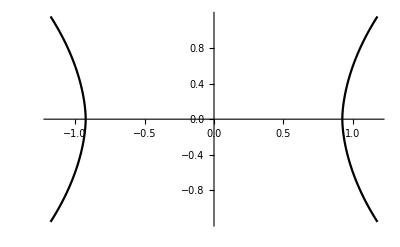

```mathematica
ListLinePlot[{PPBoundary,NPBoundary,NNBoundary,PNBoundary},PlotStyle->Black]
```

### Upper Cut Curve (LoC) in 2D

```mathematica
PPUpperCut200=CSCutCurvein2D[{0.9239453620743007,0},{1188},{200,923,1}];
NPUpperCut200=Table[{-1,1},{i,1,923}]*PPUpperCut200;
NNUpperCut200=Table[{-1,-1},{i,1,923}]*PPUpperCut200;
PNUpperCut200=Table[{1,-1},{i,1,923}]*PPUpperCut200;
```

```mathematica
PPUpperCut400=CSCutCurvein2D[{0.9239453620743007,0},{1188},{400,975,1}];
NPUpperCut400=Table[{-1,1},{i,1,975}]*PPUpperCut400;
NNUpperCut400=Table[{-1,-1},{i,1,975}]*PPUpperCut400;
PNUpperCut400=Table[{1,-1},{i,1,975}]*PPUpperCut400;
```

```mathematica
PPUpperCut600=CSCutCurvein2D[{0.9239453620743007,0},{1188},{600,1040,1}];
NPUpperCut600=Table[{-1,1},{i,1,1040}]*PPUpperCut600;
NNUpperCut600=Table[{-1,-1},{i,1,1040}]*PPUpperCut600;
PNUpperCut600=Table[{1,-1},{i,1,1040}]*PPUpperCut600;
```

```mathematica
PPUpperCut800=CSCutCurvein2D[{0.9239453620743007,0},{1188},{800,1112,1}];
NPUpperCut800=Table[{-1,1},{i,1,1112}]*PPUpperCut800;
NNUpperCut800=Table[{-1,-1},{i,1,1112}]*PPUpperCut800;
PNUpperCut800=Table[{1,-1},{i,1,1112}]*PPUpperCut800;
```

```mathematica
PPUpperCut1000=CSCutCurvein2D[{0.9239453620743007,0},{1188},{1000,1188,1}];
NPUpperCut1000=Table[{-1,1},{i,1,1188}]*PPUpperCut1000;
NNUpperCut1000=Table[{-1,-1},{i,1,1188}]*PPUpperCut1000;
PNUpperCut1000=Table[{1,-1},{i,1,1188}]*PPUpperCut1000;
```

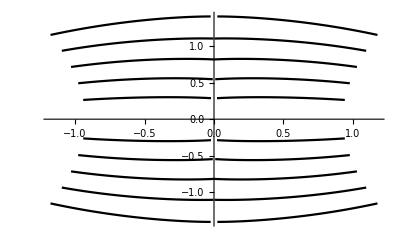

```mathematica
ListLinePlot[{
PPUpperCut200,NPUpperCut200,NNUpperCut200,PNUpperCut200,
PPUpperCut400,NPUpperCut400,NNUpperCut400,PNUpperCut400,
PPUpperCut600,NPUpperCut600,NNUpperCut600,PNUpperCut600,
PPUpperCut800,NPUpperCut800,NNUpperCut800,PNUpperCut800,
PPUpperCut1000,NPUpperCut1000,NNUpperCut1000,PNUpperCut1000},PlotStyle->Black]
```

### Lower Cut LoC in 2D

#### When u (or v) start from 0 to 200 and v (or u) is 0

```mathematica
PPLowerCut0={{0.041178617626428604,0.11031299084424973},{0.04131447523832321,0.11032817512750626},{0.04229896888136864,0.11043568700551987},{0.04326866939663887,0.11054091155529022},{0.044338081032037735,0.10965029150247574},{0.045290544629096985,0.10975202918052673},{0.046237871050834656,0.10985245555639267},{0.04718146473169327,0.10995184630155563},{0.04812229797244072,0.11005008965730667},{0.049061164259910583,0.11014731973409653},{0.0499984547495842,0.11024373024702072},{0.05093468725681305,0.11033930629491806},{0.051870156079530716,0.11043419688940048},{0.052805084735155106,0.1105281412601471},{0.05373954027891159,0.11062156409025192},{0.05467384681105614,0.1107141301035881},{0.05560803413391113,0.11080604046583176},{0.05654216185212135,0.11089742928743362},{0.05747636407613754,0.11098792403936386},{0.0584106408059597,0.11107811331748962},{0.059345126152038574,0.111167311668396},{0.0602797232568264,0.11125613003969193},{0.06121456250548363,0.11134441941976547},{0.06214965134859085,0.11143206059932709},{0.06308498233556747,0.11151900142431259},{0.06402060389518738,0.11160556972026825},{0.06495649367570877,0.11169139295816422},{0.06589271128177643,0.11177675426006317},{0.06682918220758438,0.11186157912015915},{0.06687335669994354,0.11186639219522476},{0.0678093209862709,0.11195070296525955},{0.06874571740627289,0.11203436553478241},{0.06968243420124054,0.11211757361888885},{0.07061944156885147,0.11220020055770874},{0.07155679166316986,0.11228229105472565},{0.07249446958303452,0.11236397922039032},{0.07343258708715439,0.11244523525238037},{0.07437092810869217,0.11252568662166595},{0.07530966401100159,0.11260601878166199},{0.07624867558479309,0.11268553882837296},{0.07718798518180847,0.11276472359895706},{0.07812768965959549,0.11284337937831879},{0.07906774431467056,0.1129215881228447},{0.08000801503658295,0.11299937963485718},{0.08094862103462219,0.11307661980390549},{0.08199329674243927,0.11215902119874954},{0.08293429017066956,0.11223523318767548},{0.08387558162212372,0.11231117695569992},{0.08481724560260773,0.11238662898540497},{0.08575916290283203,0.11246155202388763},{0.08670131117105484,0.11253615468740463},{0.08764373511075974,0.11261017620563507},{0.08858653903007507,0.11268400400876999},{0.08861786872148514,0.11268696933984756},{0.08956048637628555,0.11276029795408249},{0.09050341695547104,0.11283303052186966},{0.09144661575555801,0.11290525645017624},{0.09239009022712708,0.11297702044248581},{0.09333375841379166,0.1130485087633133},{0.0942777469754219,0.11311960965394974},{0.09522195905447006,0.11319026350975037},{0.09616642445325851,0.1132604330778122},{0.09711108356714249,0.11333014070987701},{0.09805605560541153,0.11339950561523438},{0.09900124371051788,0.11346842348575592},{0.09994670748710632,0.1135370135307312},{0.1008923202753067,0.11360500007867813},{0.10183823853731155,0.11367270350456238},{0.10278432071208954,0.11374010145664215},{0.1037306860089302,0.11380697786808014},{0.10467718541622162,0.1138734370470047},{0.10572372376918793,0.11294471472501755},{0.10574967414140701,0.11294728517532349},{0.10669620335102081,0.11301297694444656},{0.1076430007815361,0.11307825148105621},{0.1085900217294693,0.11314309388399124},{0.10953725874423981,0.1132076233625412},{0.11048459261655807,0.11327170580625534},{0.11143223196268082,0.11333541572093964},{0.11238006502389908,0.11339875310659409},{0.11332797259092331,0.11346174031496048},{0.1142762154340744,0.11352431029081345},{0.11522457003593445,0.11358638852834702},{0.11617320775985718,0.1136481836438179},{0.11712191253900528,0.11370981484651566},{0.11807092279195786,0.11377080529928207},{0.11901992559432983,0.11383147537708282},{0.11996925622224808,0.11389195173978806},{0.12091877311468124,0.11395179480314255},{0.12094101309776306,0.11395387351512909},{0.12189056724309921,0.11401373893022537},{0.12284012883901596,0.1140727773308754},{0.1237899586558342,0.11413160711526871},{0.12483682483434677,0.11319506913423538},{0.12578678131103516,0.11325308680534363},{0.12673692405223846,0.11331090331077576},{0.1276872605085373,0.11336826533079147},{0.12863771617412567,0.11342521756887436},{0.12958835065364838,0.11348196119070053},{0.13053910434246063,0.11353825032711029},{0.13149011135101318,0.11359438300132751},{0.1324412077665329,0.11364980787038803},{0.13339243829250336,0.11370532214641571},{0.13434375822544098,0.11376012861728668},{0.13529525697231293,0.11381474137306213},{0.1353151500225067,0.11381649225950241},{0.13626667857170105,0.1138710081577301},{0.13721832633018494,0.11392463743686676},{0.1381702423095703,0.11397826671600342},{0.1391221433877945,0.11403138190507889},{0.14007419347763062,0.11408424377441406},{0.14102651178836823,0.11413688957691193},{0.14197883009910583,0.11418896913528442},{0.14302536845207214,0.11324552446603775},{0.14397791028022766,0.11329697072505951},{0.14493054151535034,0.11334818601608276},{0.1458832174539566,0.11339911073446274},{0.1468362808227539,0.11344946920871735},{0.1477890908718109,0.11349955946207047},{0.14874225854873657,0.11354949325323105},{0.1487601399421692,0.11355100572109222},{0.14971333742141724,0.11360051482915878},{0.1506665050983429,0.11364985257387161},{0.1516198068857193,0.1136985495686531},{0.152573361992836,0.11374697834253311},{0.15352697670459747,0.11379529535770416},{0.1544807106256485,0.11384326964616776},{0.155434712767601,0.11389071494340897},{0.1563885509967804,0.11393775790929794},{0.15734262764453888,0.11398478597402573},{0.15829682350158691,0.11403149366378784},{0.15925118327140808,0.11407781392335892},{0.16029703617095947,0.11312799155712128},{0.1612512171268463,0.11317361146211624},{0.16220569610595703,0.1132190003991127},{0.16222205758094788,0.11322049796581268},{0.16317641735076904,0.1132655218243599},{0.16413110494613647,0.11331009864807129},{0.16508574783802032,0.11335460096597672},{0.1660405844449997,0.11339868605136871},{0.16699543595314026,0.11344242841005325},{0.16795048117637634,0.11348588764667511},{0.16890548169612885,0.11352887749671936},{0.1698608100414276,0.11357160657644272},{0.17081597447395325,0.11361417174339294},{0.17177145183086395,0.11365646868944168},{0.1727268397808075,0.11369835585355759},{0.1736825704574585,0.11374001204967499},{0.17463815212249756,0.11378134042024612},{0.1746530830860138,0.11378250271081924},{0.1756979078054428,0.11282780766487122},{0.1766534298658371,0.11286860704421997},{0.17760922014713287,0.11290886253118515},{0.17856499552726746,0.11294898390769958},{0.17952080070972443,0.11298882961273193},{0.1804768592119217,0.11302824318408966},{0.18143291771411896,0.11306745558977127},{0.18238912522792816,0.11310635507106781},{0.1833452582359314,0.11314483731985092},{0.1843017041683197,0.11318325251340866},{0.18525807559490204,0.1132211983203888},{0.18621453642845154,0.1132589653134346},{0.1871711015701294,0.11329641938209534},{0.1871848851442337,0.11329742521047592},{0.18814143538475037,0.11333456635475159},{0.18909822404384613,0.11337139457464218},{0.19014182686805725,0.11241211742162704},{0.19109848141670227,0.11244822293519974},{0.19205515086650848,0.11248420923948288},{0.19301211833953857,0.1125199943780899},{0.19396895170211792,0.11255540698766708},{0.19492608308792114,0.1125904843211174},{0.19588300585746765,0.11262527108192444},{0.19684015214443207,0.11265986412763596},{0.1977972537279129,0.11269405484199524},{0.1987546682357788,0.1127280592918396},{0.19876742362976074,0.1127290278673172},{0.19972461462020874,0.11276275664567947},{0.20068210363388062,0.11279613524675369},{0.20163936913013458,0.11282922327518463},{0.20259684324264526,0.1128620132803917},{0.20355446636676788,0.11289455741643906},{0.20459681749343872,0.11193080991506577},{0.20555438101291656,0.1119627058506012},{0.20651206374168396,0.11199451982975006},{0.20746970176696777,0.11202584207057953},{0.2084275484085083,0.11205698549747467},{0.20938518643379211,0.11208786070346832},{0.21034319698810577,0.11211850494146347},{0.21130111813545227,0.11214885115623474},{0.21131303906440735,0.11214985698461533},{0.21227100491523743,0.11217987537384033},{0.2132289558649063,0.11220958083868027},{0.21418699622154236,0.1122390627861023},{0.2151452749967575,0.11226838082075119},{0.21610340476036072,0.11229721456766129},{0.21706163883209229,0.11232588440179825},{0.21802006661891937,0.11235425621271133},{0.2190607786178589,0.11138618737459183},{0.22001919150352478,0.11141407489776611},{0.2209775298833847,0.11144164204597473},{0.22193601727485657,0.11146891117095947},{0.22289447486400604,0.11149589717388153},{0.2229054719209671,0.11149696260690689},{0.22386398911476135,0.11152367293834686},{0.22482247650623322,0.11155018210411072},{0.2257811427116394,0.11157642304897308},{0.22673967480659485,0.11160255968570709},{0.22769850492477417,0.11162826418876648},{0.2286570817232132,0.11165369302034378},{0.22961600124835968,0.11167877912521362},{0.2305748015642166,0.1117037981748581},{0.23153357207775116,0.11172831058502197},{0.23257321119308472,0.11075635254383087},{0.23353202641010284,0.1107805147767067},{0.2344910204410553,0.11080466955900192},{0.23450130224227905,0.11080539971590042},{0.23546019196510315,0.11082885414361954},{0.23641906678676605,0.11085215955972672},{0.2373780459165573,0.11087535321712494},{0.23833726346492767,0.11089815199375153},{0.2392963021993637,0.11092063784599304},{0.24025554955005646,0.1109432652592659},{0.24121470749378204,0.11096520721912384},{0.2421739399433136,0.11098704487085342},{0.24313317239284515,0.11100863665342331},{0.2440926432609558,0.11102989315986633},{0.24513062834739685,0.11005445569753647},{0.24514026939868927,0.11005514860153198},{0.246099591255188,0.11007589101791382},{0.24705873429775238,0.11009629815816879},{0.24801813066005707,0.11011659353971481},{0.2489774525165558,0.11013659834861755},{0.24993692338466644,0.11015651375055313},{0.2508963644504547,0.11017594486474991},{0.25185590982437134,0.11019514501094818},{0.2528153359889984,0.11021415144205093},{0.25377508997917175,0.11023300141096115},{0.25473472476005554,0.11025157570838928},{0.2556944489479065,0.11026975512504578},{0.25665414333343506,0.11028767377138138},{0.2566629946231842,0.11028838157653809},{0.257699579000473,0.10930948704481125},{0.25865912437438965,0.10932692885398865},{0.25961872935295105,0.10934409499168396},{0.2605783939361572,0.1093612089753151},{0.26153814792633057,0.10937803238630295},{0.26249799132347107,0.10939464718103409},{0.2634578049182892,0.10941077023744583},{0.26441729068756104,0.10942680388689041},{0.26537734270095825,0.10944267362356186},{0.2663373053073883,0.10945805162191391},{0.26729726791381836,0.1094733476638794},{0.26825734972953796,0.10948850214481354},{0.26826566457748413,0.10948897898197174},{0.26930078864097595,0.10850696265697479},{0.27026069164276123,0.10852150619029999},{0.27122047543525696,0.1085357815027237},{0.2721802890300751,0.1085498258471489},{0.27314022183418274,0.108563631772995},{0.2741002142429352,0.10857720673084259},{0.2750602662563324,0.10859072953462601},{0.2760203182697296,0.10860369354486465},{0.2769804298877716,0.10861660540103912},{0.2779408097267151,0.10862912237644196},{0.27890077233314514,0.10864138603210449},{0.27890855073928833,0.1086418479681015},{0.27986887097358704,0.10865414887666702},{0.2808290421962738,0.10866605490446091},{0.2818623185157776,0.10768071562051773},{0.28282251954078674,0.10769212990999222},{0.28378239274024963,0.10770325362682343},{0.2847428321838379,0.10771435499191284},{0.28570306301116943,0.10772493481636047},{0.2866634726524353,0.10773541033267975},{0.2876233756542206,0.10774563252925873},{0.28858381509780884,0.10775560885667801},{0.2895439565181732,0.10776537656784058},{0.28955143690109253,0.10776574909687042},{0.290511816740036,0.10777536034584045},{0.29147180914878845,0.1077846884727478},{0.2924325466156006,0.10779371112585068},{0.2934642732143402,0.1068054735660553},{0.29442429542541504,0.10681404918432236},{0.2953847050666809,0.10682238638401031},{0.29634523391723633,0.10683060437440872},{0.2973054349422455,0.10683847218751907},{0.298265665769577,0.1068459153175354},{0.29922622442245483,0.10685329884290695},{0.30018651485443115,0.10686055570840836},{0.3011470437049866,0.10686752200126648},{0.30115368962287903,0.10686784982681274},{0.302114337682724,0.10687463730573654},{0.3030747175216675,0.10688107460737228},{0.30403515696525574,0.10688735544681549},{0.3050653040409088,0.10589613765478134},{0.30602580308914185,0.10590209066867828},{0.3069862425327301,0.10590748488903046},{0.3079463839530945,0.10591280460357666},{0.308907151222229,0.10591789335012436},{0.3098676800727844,0.10592278093099594},{0.31082791090011597,0.10592736303806305},{0.3117886781692505,0.10593176633119583},{0.3117949366569519,0.10593216121196747},{0.31275543570518494,0.10593631118535995},{0.31371602416038513,0.10594026744365692},{0.3146764636039734,0.10594405233860016},{0.31563717126846313,0.10594754666090012},{0.3166656494140625,0.10495355725288391},{0.3176261782646179,0.10495664924383163},{0.3185864984989166,0.10495944321155548},{0.31954702734947205,0.10496197640895844},{0.32050737738609314,0.10496440529823303},{0.3214680850505829,0.10496651381254196},{0.3224286139011383,0.10496852546930313},{0.32243454456329346,0.10496877133846283},{0.32339513301849365,0.10497044026851654},{0.3243556618690491,0.10497204214334488},{0.32531604170799255,0.10497317463159561},{0.32627683877944946,0.10497424006462097},{0.32730385661125183,0.1039777621626854},{0.3282642066478729,0.10397837311029434},{0.3292247951030731,0.10397858917713165},{0.3301853537559509,0.10397882759571075},{0.33114585280418396,0.1039787083864212},{0.33210641145706177,0.10397843271493912},{0.3330667316913605,0.10397789627313614},{0.33307233452796936,0.10397819429636002},{0.3340330123901367,0.10397752374410629},{0.33499351143836975,0.10397645086050034},{0.3359537720680237,0.10397525131702423},{0.33691465854644775,0.10397379100322723},{0.3378751575946808,0.10397229343652725},{0.33890068531036377,0.10297306627035141},{0.3398609757423401,0.1029709205031395},{0.3408214747905731,0.10296855121850967},{0.3417817950248718,0.10296608507633209},{0.34274253249168396,0.10296344757080078},{0.34370318055152893,0.10296044498682022},{0.3437081277370453,0.10296069830656052},{0.3446686863899231,0.10295742750167847},{0.3456292748451233,0.10295414179563522},{0.34658992290496826,0.10295051336288452},{0.34755033254623413,0.1029467061161995},{0.3485110104084015,0.10294266790151596},{0.3495346009731293,0.10194081813097},{0.35049495100975037,0.10193642973899841},{0.35145553946495056,0.10193175077438354},{0.35241609811782837,0.10192687064409256},{0.35337668657302856,0.10192158818244934},{0.3543368875980377,0.10191646218299866},{0.35434186458587646,0.10191670060157776},{0.35530203580856323,0.10191097110509872},{0.3562626838684082,0.1019052267074585},{0.35722318291664124,0.10189928859472275},{0.35818371176719666,0.10189317911863327},{0.35914433002471924,0.10188663005828857},{0.36016643047332764,0.10088253766298294},{0.3611266613006592,0.10087557137012482},{0.3620871305465698,0.10086851567029953},{0.36304768919944763,0.10086117684841156},{0.3640078902244568,0.10085372626781464},{0.36496853828430176,0.10084604471921921},{0.36497294902801514,0.10084628313779831},{0.3659331202507019,0.10083839297294617},{0.36689358949661255,0.10083020478487015},{0.3678539991378784,0.10082173347473145},{0.368814617395401,0.10081333667039871},{0.36983492970466614,0.09980682283639908},{0.37079527974128723,0.09979784488677979},{0.3717554211616516,0.09978868067264557},{0.3727160692214966,0.09977931529283524},{0.37367624044418335,0.09976963698863983},{0.37463676929473877,0.09975988417863846},{0.37559717893600464,0.09974981844425201},{0.3756009042263031,0.09974996000528336},{0.37656134366989136,0.09973983466625214},{0.37752193212509155,0.09972947835922241},{0.3784818649291992,0.09971863031387329},{0.3794423043727875,0.09970784932374954},{0.3804610073566437,0.0986989215016365},{0.38142138719558716,0.09868764132261276},{0.38238146901130676,0.09867598861455917},{0.38334164023399353,0.09866440296173096},{0.3843018412590027,0.09865245223045349},{0.38526228070259094,0.09864041209220886},{0.38622257113456726,0.09862802922725677},{0.38622602820396423,0.09862818568944931},{0.38718611001968384,0.09861567616462708},{0.38814663887023926,0.09860315918922424},{0.3891068994998932,0.09858991950750351},{0.39006727933883667,0.0985768511891365},{0.3910841643810272,0.09756560623645782},{0.39204397797584534,0.0975520983338356},{0.3930043876171112,0.09753817319869995},{0.3939642310142517,0.09752427041530609},{0.394924521446228,0.09751001000404358},{0.39588460326194763,0.0974956750869751},{0.3958877921104431,0.09749585390090942},{0.39684808254241943,0.09748110920190811},{0.39780813455581665,0.09746623039245605},{0.3987683057785034,0.09745150059461594},{0.3997284173965454,0.09743618965148926},{0.40074384212493896,0.09642284363508224},{0.40170368552207947,0.09640710800886154},{0.4026634693145752,0.09639131277799606},{0.40362364053726196,0.09637520462274551},{0.4045833647251129,0.09635899215936661},{0.4055435359477997,0.09634251147508621},{0.406503289937973,0.09632580727338791},{0.40650635957717896,0.09632597863674164},{0.4074663519859314,0.09630919247865677},{0.408426433801651,0.09629200398921967},{0.4093863070011139,0.09627486020326614},{0.410399854183197,0.09525923430919647},{0.4113596975803375,0.09524161368608475},{0.41231951117515564,0.09522368758916855},{0.4132794141769409,0.09520555287599564},{0.4142393171787262,0.09518737345933914},{0.4151992201805115,0.09516893327236176},{0.4161587655544281,0.09515022486448288},{0.41711854934692383,0.09513141959905624},{0.4171213209629059,0.09513145685195923},{0.41808101534843445,0.09511235356330872},{0.4190407395362854,0.09509314596652985},{0.42000070214271545,0.09507357329130173},{0.4210125207901001,0.09405560791492462},{0.4219718873500824,0.09403582662343979},{0.4229317605495453,0.09401572495698929},{0.4238913059234619,0.09399539232254028},{0.4248512089252472,0.09397497028112411},{0.4258106052875519,0.0939541682600975},{0.4267702102661133,0.09393338859081268},{0.4267726540565491,0.09393350034952164},{0.42773231863975525,0.09391220659017563},{0.42869195342063904,0.09389092773199081},{0.4296514391899109,0.09386955201625824},{0.4306614398956299,0.09284963458776474},{0.43162110447883606,0.09282775968313217},{0.4325803816318512,0.09280556440353394},{0.4335396885871887,0.0927833542227745},{0.43449923396110535,0.09276091307401657},{0.43545886874198914,0.09273821860551834},{0.43641799688339233,0.09271522611379623},{0.4373777210712433,0.09269226342439651},{0.43737953901290894,0.0926923006772995},{0.43833911418914795,0.09266898036003113},{0.43929851055145264,0.09264561533927917},{0.440306693315506,0.09162361919879913},{0.44126614928245544,0.09159968793392181},{0.44222530722618103,0.09157566726207733},{0.443184494972229,0.09155140072107315},{0.44414371252059937,0.09152691066265106},{0.44510307908058167,0.09150222688913345},{0.44606226682662964,0.09147749096155167},{0.447021484375,0.09145244210958481},{0.44798076152801514,0.09142717719078064},{0.4479825496673584,0.09142719954252243},{0.4489419460296631,0.09140174090862274},{0.4499482214450836,0.0903778001666069},{0.4509073495864868,0.090351901948452},{0.45186617970466614,0.0903259813785553},{0.4528252184391022,0.09029962867498398},{0.4537845849990845,0.09027319401502609},{0.4547431468963623,0.09024662524461746},{0.45570236444473267,0.09021979570388794},{0.4566613435745239,0.09019280970096588},{0.4576205611228943,0.09016551077365875},{0.4576220214366913,0.09016551077365875},{0.4586270749568939,0.08913973718881607},{0.45958539843559265,0.08911216259002686},{0.46054449677467346,0.08908448368310928},{0.4615030586719513,0.0890563428401947},{0.46246206760406494,0.08902822434902191},{0.4634205996990204,0.08899980783462524},{0.4643798768520355,0.08897136896848679},{0.46533840894699097,0.0889425128698349},{0.4662972390651703,0.08891347795724869},{0.4672558605670929,0.08888445794582367},{0.46821483969688416,0.0888550877571106},{0.4682605266571045,0.08785656839609146},{0.4692187011241913,0.08782713860273361},{0.47017747163772583,0.08779735118150711},{0.4711359739303589,0.08776748925447464},{0.4720945358276367,0.08773726969957352},{0.4730531871318817,0.08770702034235},{0.4740116596221924,0.08767665922641754},{0.474970281124115,0.08764582872390747},{0.47592878341674805,0.0876149982213974},{0.4768873155117035,0.08758388459682465},{0.47784584760665894,0.08755268156528473},{0.47788962721824646,0.08655407279729843},{0.47884801030158997,0.086522676050663},{0.47980639338493347,0.08649091422557831},{0.4807645082473755,0.08645912259817123},{0.48172304034233093,0.08642701059579849},{0.48268115520477295,0.0863947868347168},{0.4836394786834717,0.08636237680912018},{0.4845978915691376,0.08632971346378326},{0.4855559468269348,0.08629699051380157},{0.4865143895149231,0.08626404404640198},{0.48751357197761536,0.08523225784301758},{0.4884719252586365,0.08519880473613739},{0.4884725511074066,0.08519880473613739},{0.48943039774894714,0.08516527712345123},{0.4903887212276459,0.08513150364160538},{0.4913465678691864,0.0850975438952446},{0.49230483174324036,0.0850633829832077},{0.4932626187801361,0.08502910286188126},{0.4942208230495453,0.08499449491500854},{0.4951787292957306,0.08495981246232986},{0.4961366653442383,0.08492487668991089},{0.49713441729545593,0.08389126509428024},{0.4980922043323517,0.08385591953992844},{0.49809256196022034,0.08385595679283142},{0.49905046820640564,0.0838204100728035},{0.5000081062316895,0.08378487080335617},{0.5009660720825195,0.0837489664554596},{0.5019237399101257,0.08371293544769287},{0.5028814077377319,0.08367668092250824},{0.5038394927978516,0.0836402177810669},{0.5047966241836548,0.08360365778207779},{0.5057926774024963,0.08256803452968597},{0.5067507028579712,0.08253124356269836},{0.5077077746391296,0.08249390870332718},{0.5086652636528015,0.08245664089918137},{0.5086654424667358,0.08245663344860077},{0.5096227526664734,0.08241905272006989},{0.5105809569358826,0.08238132297992706},{0.5115380883216858,0.08234342187643051},{0.5124951004981995,0.08230546116828918},{0.5134527683258057,0.0822669193148613},{0.5144105553627014,0.08222854137420654},{0.5154039859771729,0.08119099587202072},{0.5163614153862,0.08115221560001373},{0.517318844795227,0.08111311495304108},{0.5182768106460571,0.08107387274503708},{0.5182767510414124,0.08107385784387589},{0.5192327499389648,0.08103445917367935},{0.5201901197433472,0.08099478483200073},{0.5211477875709534,0.08095506578683853},{0.5221052169799805,0.08091504871845245},{0.5230615139007568,0.080874964594841},{0.5240545868873596,0.07983559370040894},{0.5250112414360046,0.07979506999254227},{0.5259677171707153,0.07975437492132187},{0.5269246101379395,0.07971345633268356},{0.5278818011283875,0.07967230677604675},{0.5288388133049011,0.07963114231824875},{0.5288386344909668,0.07963110506534576},{0.5297954082489014,0.07958948612213135},{0.5307518243789673,0.07954791188240051},{0.5317089557647705,0.0795060321688652},{0.5327001810073853,0.07846511900424957},{0.5336562991142273,0.07842285931110382},{0.5346125960350037,0.07838048040866852},{0.5355693697929382,0.07833778858184814},{0.536526620388031,0.07829508185386658},{0.537482500076294,0.07825201004743576},{0.5384389162063599,0.07820911705493927},{0.5384382605552673,0.07820910215377808},{0.5393952131271362,0.07816572487354279},{0.5403522253036499,0.07812204211950302},{0.5413403511047363,0.07707938551902771},{0.5422971844673157,0.07703559845685959},{0.5432535409927368,0.07699139416217804},{0.5442097187042236,0.0769471675157547},{0.5451658964157104,0.07690289616584778},{0.5461220741271973,0.07685805857181549},{0.5470786690711975,0.076813243329525},{0.54803466796875,0.07676829397678375},{0.5489910244941711,0.07672315090894699},{0.5489903688430786,0.0767231434583664},{0.5499774217605591,0.07567869871854782},{0.5509330630302429,0.07563329488039017},{0.5518894791603088,0.0755874440073967},{0.5528460144996643,0.07554148882627487},{0.5538012385368347,0.07549544423818588},{0.5547570586204529,0.07544908672571182},{0.5557129979133606,0.07540277391672134},{0.5566690564155579,0.07535602152347565},{0.5576251149177551,0.07530922442674637},{0.5585810542106628,0.07526206225156784},{0.5586093664169312,0.07426303625106812},{0.5595646500587463,0.07421586662530899},{0.5605211853981018,0.07416844367980957},{0.561476469039917,0.07412093132734299},{0.5624317526817322,0.07407313585281372},{0.5633875131607056,0.0740252286195755},{0.5643435120582581,0.07397706061601639},{0.5652993321418762,0.07392871379852295},{0.5662539601325989,0.07388041168451309},{0.5672099590301514,0.07383165508508682},{0.5681657791137695,0.07378295063972473},{0.5681918263435364,0.07278382033109665},{0.5691478252410889,0.07273458689451218},{0.5701030492782593,0.07268541306257248},{0.5710580945014954,0.07263586670160294},{0.572013258934021,0.07258643209934235},{0.5729685425758362,0.07253652811050415},{0.5739243030548096,0.07248672097921371},{0.5748795866966248,0.0724366083741188},{0.5758341550827026,0.07238619774580002},{0.5768159031867981,0.07133661955595016},{0.5777711868286133,0.07128594070672989},{0.5787259340286255,0.07123512029647827},{0.5787248015403748,0.07123512029647827},{0.5796793699264526,0.07118407636880875},{0.5806345343589783,0.07113291323184967},{0.5815894603729248,0.07108141481876373},{0.5825445652008057,0.07102975249290466},{0.5834990739822388,0.07097798585891724},{0.5844541788101196,0.07092610746622086},{0.5854334235191345,0.06987480819225311},{0.5863886475563049,0.06982241570949554},{0.5873432755470276,0.0697699636220932},{0.5882975459098816,0.06971723586320877},{0.5882956981658936,0.06971722096204758},{0.5892507433891296,0.06966431438922882},{0.5902055501937866,0.06961126625537872},{0.5911601185798645,0.06955814361572266},{0.5921149849891663,0.0695047527551651},{0.5930688977241516,0.06945120543241501},{0.5940464735031128,0.06839810311794281},{0.595001220703125,0.06834421306848526},{0.5959552526473999,0.06829001009464264},{0.596909761428833,0.06823579221963882},{0.597863495349884,0.06818128377199173},{0.5988180637359619,0.06812674552202225},{0.5988160967826843,0.06812671571969986},{0.5997709035873413,0.068071648478508},{0.6007251143455505,0.06801673024892807},{0.6016785502433777,0.06796145439147949},{0.6026548743247986,0.06690684705972672},{0.6036086082458496,0.06685129553079605},{0.6045630574226379,0.06679563969373703},{0.6055167317390442,0.06673967093229294},{0.6064705848693848,0.06668350845575333},{0.6074241995811462,0.06662722676992416},{0.6083781123161316,0.06657078862190247},{0.6083763241767883,0.06657079607248306},{0.6093304753303528,0.06651410460472107},{0.6102842092514038,0.06645740568637848},{0.6112580299377441,0.06540093570947647},{0.6122114062309265,0.06534387916326523},{0.6131650805473328,0.0652862936258316},{0.6141191124916077,0.06522884219884872},{0.6150721311569214,0.06517098844051361},{0.6160256266593933,0.06511320918798447},{0.6169790029525757,0.06505507230758667},{0.6179327368736267,0.0649968832731247},{0.6188862323760986,0.06493838131427765},{0.6188842058181763,0.06493834406137466},{0.6198558807373047,0.06388042867183685},{0.6208093166351318,0.06382168084383011},{0.6217625737190247,0.06376254558563232},{0.6227155327796936,0.06370353698730469},{0.6236692667007446,0.06364411860704422},{0.6246214509010315,0.06358468532562256},{0.6255749464035034,0.06352479755878448},{0.6265281438827515,0.06346509605646133},{0.62748122215271,0.06340493261814117},{0.6284509897232056,0.062345534563064575},{0.6284488439559937,0.0623454786837101},{0.6294013857841492,0.06228495389223099},{0.6303548812866211,0.062224484980106354},{0.6313073635101318,0.062163542956113815},{0.6322603225708008,0.06210263818502426},{0.6332123279571533,0.06204143539071083},{0.634165346622467,0.06198016181588173},{0.6351187229156494,0.06191852688789368},{0.6360707879066467,0.061857059597969055},{0.6370391249656677,0.060795851051807404},{0.6379916071891785,0.06073374301195145},{0.6379887461662292,0.06073375791311264},{0.6389416456222534,0.06067170947790146},{0.6398942470550537,0.06060921028256416},{0.6408465504646301,0.06054672598838806},{0.6417984366416931,0.06048388034105301},{0.6427507400512695,0.060421139001846313},{0.6437035202980042,0.06035786494612694},{0.6446555256843567,0.06029466167092323},{0.6456220746040344,0.0592317059636116},{0.6465738415718079,0.05916821211576462},{0.6475257873535156,0.059104323387145996},{0.6484783887863159,0.05904040113091469},{0.6484754085540771,0.05904039740562439},{0.6494272351264954,0.058976273983716965},{0.6503793597221375,0.05891188979148865},{0.6513312458992004,0.05884725600481033},{0.6522829532623291,0.058782629668712616},{0.653235137462616,0.05871781334280968},{0.6541990041732788,0.0576532706618309},{0.6551508903503418,0.05758821219205856},{0.6561025977134705,0.05752253532409668},{0.6570543646812439,0.05745712295174599},{0.6580060720443726,0.05739118903875351},{0.6580026745796204,0.057391226291656494},{0.6589546203613281,0.057325538247823715},{0.659905731678009,0.05725928395986557},{0.6608578562736511,0.05719320476055145},{0.6618199944496155,0.05612704157829285},{0.6627715229988098,0.05606047809123993},{0.6637225151062012,0.055993545800447464},{0.6646740436553955,0.05592662841081619},{0.6656253933906555,0.05585933104157448},{0.6665756702423096,0.05579210817813873},{0.6675270199775696,0.05572439357638359},{0.6684784889221191,0.05565672740340233},{0.6684752106666565,0.05565677955746651},{0.6694268584251404,0.05558890849351883},{0.6703870296478271,0.05452141910791397},{0.6713380813598633,0.05445319041609764},{0.672289252281189,0.05438484624028206},{0.6732398271560669,0.05431618541479111},{0.6741902828216553,0.05424727872014046},{0.6751413345336914,0.054178547114133835},{0.676091730594635,0.05410918593406677},{0.6770429015159607,0.05404004827141762},{0.6779939532279968,0.05397048592567444},{0.6779981255531311,0.05297107622027397},{0.6789489984512329,0.052901461720466614},{0.6798991560935974,0.0528314970433712},{0.6808492541313171,0.05276154354214668},{0.6818000078201294,0.05269131064414978},{0.68274986743927,0.05262116715312004},{0.6837008595466614,0.052550435066223145},{0.6846511363983154,0.052479684352874756},{0.6856012344360352,0.05240878462791443},{0.6865514516830444,0.05233779549598694},{0.6875084638595581,0.0512671023607254},{0.6884579062461853,0.0511956624686718},{0.6884543895721436,0.05119568482041359},{0.6894046068191528,0.05112409591674805},{0.6903547644615173,0.051052264869213104},{0.6913048028945923,0.050980474799871445},{0.6922544240951538,0.050908222794532776},{0.6932045221328735,0.05083593353629112},{0.694153904914856,0.050763390958309174},{0.6951085329055786,0.04969128221273422},{0.6960586309432983,0.04961837828159332},{0.6970080733299255,0.049545448273420334},{0.6979577541351318,0.04947223141789436},{0.6979544162750244,0.04947236180305481},{0.6989043354988098,0.0493989959359169},{0.6998528838157654,0.04932548850774765},{0.7008025646209717,0.04925166442990303},{0.7017524242401123,0.049177709966897964},{0.7027013301849365,0.04910369589924812},{0.7036537528038025,0.04803008586168289},{0.7046038508415222,0.047955598682165146},{0.7055525779724121,0.047881096601486206},{0.7065017819404602,0.04780621454119682},{0.7074508666992188,0.0477314293384552},{0.7084001302719116,0.047656308859586716},{0.7083960175514221,0.047656286507844925},{0.7093451619148254,0.04758097231388092},{0.710293710231781,0.04750533774495125},{0.711245059967041,0.0464303158223629},{0.7121938467025757,0.046354543417692184},{0.7131428122520447,0.04627855494618416},{0.7140914797782898,0.04620244726538658},{0.7150402665138245,0.04612601548433304},{0.715988278388977,0.046049512922763824},{0.7169373035430908,0.045972853899002075},{0.7178864479064941,0.04589591920375824},{0.7178818583488464,0.0458960123360157},{0.7188307046890259,0.045818861573934555},{0.7197797894477844,0.04474226385354996},{0.720727801322937,0.044664718210697174},{0.7216758131980896,0.04458733648061752},{0.7226240634918213,0.04450951889157295},{0.7235724329948425,0.04443163052201271},{0.7245206832885742,0.0443534180521965},{0.7254689931869507,0.044275280088186264},{0.7264166474342346,0.044196728616952896},{0.7273654937744141,0.044118162244558334},{0.7283121347427368,0.043039750307798386},{0.7283076047897339,0.04303984344005585},{0.7292559742927551,0.04296096786856651},{0.7302034497261047,0.04288170486688614},{0.7311509251594543,0.042802438139915466},{0.732099175453186,0.04272301122546196},{0.7330470085144043,0.04264331981539726},{0.7339946627616882,0.042563460767269135},{0.7349418997764587,0.04248341545462608},{0.7358901500701904,0.0424032062292099},{0.7368343472480774,0.0413232184946537},{0.7377820014953613,0.04124274104833603},{0.737777829170227,0.04124285280704498},{0.7387247085571289,0.04116200655698776},{0.7396721243858337,0.04108119010925293},{0.7406200170516968,0.04100004956126213},{0.7415674328804016,0.040918853133916855},{0.7425137162208557,0.04083731770515442},{0.7434618473052979,0.04075594246387482},{0.7444042563438416,0.03967456892132759},{0.7453515529632568,0.039592575281858444},{0.746298611164093,0.039510563015937805},{0.7472447156906128,0.03942820057272911},{0.7481921911239624,0.03934576362371445},{0.7481878399848938,0.03934577852487564},{0.7491343021392822,0.03926311060786247},{0.750080943107605,0.039180342108011246},{0.7510278224945068,0.03909727931022644},{0.7519751787185669,0.039014190435409546},{0.7529152035713196,0.037931255996227264},{0.7538623809814453,0.03784770891070366},{0.754808247089386,0.03776410222053528},{0.7557545900344849,0.03768019750714302},{0.7567017078399658,0.03759609907865524},{0.7576471567153931,0.03751186281442642},{0.7576431632041931,0.037511955946683884},{0.7585892677307129,0.037427593022584915},{0.7595357298851013,0.03734305500984192},{0.760475218296051,0.03625888004899025},{0.7614203691482544,0.036173850297927856},{0.7623663544654846,0.03608890622854233},{0.7633126378059387,0.03600360453128815},{0.7642583847045898,0.03591810166835785},{0.7652042508125305,0.035832472145557404},{0.7661503553390503,0.035746678709983826},{0.767096221446991,0.03566073626279831},{0.7680416107177734,0.03557462990283966},{0.7680279612541199,0.0345752127468586},{0.7689737677574158,0.034488923847675323},{0.7699195146560669,0.034402426332235336},{0.770864725112915,0.034315746277570724},{0.7718104124069214,0.034228887408971786},{0.7727558612823486,0.0341419093310833},{0.7737013697624207,0.0340547114610672},{0.7746464014053345,0.03396741300821304},{0.7755926251411438,0.03387985751032829},{0.7765375375747681,0.03379208594560623},{0.7774723768234253,0.03270471841096878},{0.7784168720245361,0.03261668235063553},{0.7784120440483093,0.03261679410934448},{0.779357373714447,0.0325285866856575},{0.7803018689155579,0.032440170645713806},{0.7812473177909851,0.032351598143577576},{0.7821924090385437,0.032262906432151794},{0.7831374406814575,0.03217389062047005},{0.7840818166732788,0.032084871083498},{0.7850143313407898,0.030996037647128105},{0.7859591245651245,0.030906541272997856},{0.7869031429290771,0.030817007645964622},{0.7878482341766357,0.03072710521519184},{0.7878429889678955,0.03072723187506199},{0.7887877225875854,0.030637459829449654},{0.789732038974762,0.03054710291326046},{0.7906768918037415,0.030456895008683205},{0.7916208505630493,0.03036625124514103},{0.7925516366958618,0.029276225715875626},{0.7934958338737488,0.029185349121689796},{0.7944401502609253,0.029094355180859566},{0.7953837513923645,0.029003193601965904},{0.7963279485702515,0.028911719098687172},{0.7972725033760071,0.028820371255278587},{0.7982156276702881,0.02872849814593792},{0.7982110381126404,0.028728732839226723},{0.799155592918396,0.02863684669137001},{0.8000985383987427,0.028544938191771507},{0.8010268807411194,0.02745302952826023},{0.8019707798957825,0.027360811829566956},{0.802914023399353,0.02726799249649048},{0.8038576245307922,0.027175351977348328},{0.8048015832901001,0.027082709595561028},{0.8057454228401184,0.026989156380295753},{0.8066888451576233,0.02689618617296219},{0.8076323866844177,0.026802493259310722},{0.8076266646385193,0.026802681386470795},{0.8085527420043945,0.025709670037031174},{0.8094964623451233,0.025615934282541275},{0.8104392290115356,0.0255217757076025},{0.8113822937011719,0.025427954271435738},{0.8123257756233215,0.02533327229321003},{0.8132686614990234,0.02523893676698208},{0.8142114281654358,0.025144167244434357},{0.815155029296875,0.02504940703511238},{0.8160978555679321,0.024954678490757942},{0.8170217275619507,0.023859737440943718},{0.8179641366004944,0.023764509707689285},{0.8179587721824646,0.023764681071043015},{0.8189012408256531,0.023668954148888588},{0.8198443651199341,0.023573288694024086},{0.8207865357398987,0.023477809503674507},{0.8217290639877319,0.023381270468235016},{0.8226717710494995,0.02328527346253395},{0.8236148953437805,0.023188646882772446},{0.8245567679405212,0.02309216931462288},{0.8254778385162354,0.02199629321694374},{0.826421320438385,0.021898996084928513},{0.8273623585700989,0.02180211991071701},{0.8283050060272217,0.02170471101999283},{0.8282991647720337,0.021704893559217453},{0.8292415142059326,0.021607443690299988},{0.8301839232444763,0.021510040387511253},{0.8311256766319275,0.021412022411823273},{0.8320674896240234,0.021314134821295738},{0.8329868912696838,0.02021670900285244},{0.8339282870292664,0.020118245854973793},{0.8348708748817444,0.02001987397670746},{0.8358114361763,0.019921131432056427},{0.8367534875869751,0.01982232928276062},{0.8376945853233337,0.01972333714365959},{0.8386363983154297,0.019623897969722748},{0.8386312127113342,0.019624190405011177},{0.839572012424469,0.01952492445707321},{0.8405137062072754,0.01942540891468525},{0.8414308428764343,0.018326297402381897},{0.8423721194267273,0.018226459622383118},{0.8433136343955994,0.018126267939805984},{0.8442548513412476,0.018026119098067284},{0.8451956510543823,0.017925772815942764},{0.8461365699768066,0.017825113609433174},{0.8470773696899414,0.01772436685860157},{0.848018229007721,0.017623359337449074},{0.8480126857757568,0.017623569816350937},{0.8489278554916382,0.016523385420441628},{0.8498685956001282,0.016422200947999954},{0.8508096933364868,0.016320517286658287},{0.85174959897995,0.016218923032283783},{0.852690577507019,0.016117218881845474},{0.8536304235458374,0.01601518876850605},{0.8545715808868408,0.01591307483613491},{0.8555118441581726,0.015810586512088776},{0.8564526438713074,0.015708085149526596},{0.8573647141456604,0.01460640411823988},{0.8583055138587952,0.01450345292687416},{0.8582994341850281,0.014503628015518188},{0.8592396974563599,0.01440061628818512},{0.86017906665802,0.014297453686594963},{0.8611190319061279,0.014194161631166935},{0.8620590567588806,0.01409058552235365},{0.8629996180534363,0.013986952602863312},{0.8639388680458069,0.01388289500027895},{0.8648790121078491,0.0137789286673069},{0.8657900094985962,0.012675571255385876},{0.8667296171188354,0.012571034952998161},{0.8676690459251404,0.012466400861740112},{0.8686088919639587,0.012361861765384674},{0.8686023354530334,0.012362169101834297},{0.8695417046546936,0.01225711777806282},{0.8704819083213806,0.01215188205242157},{0.8714205622673035,0.012046627700328827},{0.8723596930503845,0.011941223405301571},{0.8732686042785645,0.010836450383067131},{0.8742074966430664,0.010730638168752193},{0.875146210193634,0.010624654591083527},{0.8760855197906494,0.010518624447286129},{0.8770246505737305,0.01041225716471672},{0.8779634833335876,0.010305704548954964},{0.8789023756980896,0.010198991745710373},{0.8788962960243225,0.01019931398332119},{0.8798350095748901,0.010092649608850479},{0.8807409405708313,0.008986386470496655},{0.8816801905632019,0.008879167027771473},{0.8826185464859009,0.008771839551627636},{0.8835566639900208,0.00866427831351757},{0.884495198726654,0.008556555956602097},{0.885434091091156,0.008448697626590729},{0.8863722681999207,0.008340608328580856},{0.8873112201690674,0.00823246780782938},{0.888248860836029,0.008123931474983692},{0.8891870975494385,0.008015245199203491},{0.8891465663909912,0.0070165968500077724},{0.8900846242904663,0.006908003706485033},{0.8910225629806519,0.006799006834626198},{0.8919602036476135,0.006689811125397682},{0.8928981423377991,0.0065805139020085335},{0.8938357830047607,0.0064712087623775005},{0.8947739005088806,0.006361472420394421},{0.8957123160362244,0.006251607555896044},{0.896649181842804,0.006141670513898134},{0.8975507020950317,0.005032557062804699},{0.8984881639480591,0.004922199994325638},{0.8994263410568237,0.004811713006347418},{0.8994191884994507,0.0048120529390871525},{0.900357186794281,0.004701508674770594},{0.9012944102287292,0.004590510856360197},{0.9022310972213745,0.004479447845369577},{0.9031684398651123,0.004368350375443697},{0.9041054248809814,0.004256935324519873},{0.9050055146217346,0.0031464509665966034},{0.9059423804283142,0.003034712979570031},{0.9068790674209595,0.0029228762723505497},{0.9078157544136047,0.0028107669204473495},{0.9087523221969604,0.002698503201827407},{0.9087462425231934,0.002698875032365322},{0.9096831679344177,0.002586672082543373},{0.9106203317642212,0.0024738707579672337},{0.9115560054779053,0.0023610717616975307},{0.9124921560287476,0.0022482387721538544},{0.913390040397644,0.0011362178483977914},{0.9143267869949341,0.0010229261824861169},{0.9152624011039734,0.0009094710694625974},{0.9161988496780396,0.000795934465713799},{0.9171350002288818,0.000682107056491077},{0.9180711507797241,0.0005679648602381349},{0.919007420539856,0.00045403605327010155},{0.9190005660057068,0.00045431999024003744}};
NPLowerCut0=Table[{-1,1},{i,1,1001}]*PPLowerCut0;
NNLowerCut0=Table[{-1,-1},{i,1,1001}]*PPLowerCut0;
PNLowerCut0=Table[{1,-1},{i,1,1001}]*PPLowerCut0;
```

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{0,894},{200,923},{0,160},1]
```

{{0.0411786,0.110313},{0.0413145,0.110328},{0.042299,0.110436},{0.0432687,0.110541},{0.0443381,0.10965},{0.0452905,0.109752},{0.0462379,0.109852},{0.0471815,0.109952},{0.0481223,0.11005},{0.0490612,0.110147},{0.0499985,0.110244},{0.0509347,0.110339},{0.0518702,0.110434},{0.0528051,0.110528},{0.0537395,0.110622},{0.0546738,0.110714},{0.055608,0.110806},{0.0565422,0.110897},{0.0574764,0.110988},{0.0584106,0.111078},{0.0593451,0.111167},{0.0602797,0.111256},{0.0612146,0.111344},{0.0621497,0.111432},{0.063085,0.111519},{0.0640206,0.111606},{0.0649565,0.111691},{0.0658927,0.111777},{0.0668292,0.111862},{0.0668734,0.111866},{0.0678093,0.111951},{0.0687457,0.112034},{0.0696824,0.112118},{0.0706194,0.1122},{0.0715568,0.112282},{0.0724945,0.112364},{0.0734326,0.112445},{0.0743709,0.112526},{0.0753097,0.112606},{0.0762487,0.112686},{0.077188,0.112765},{0.0781277,0.112843},{0.0790677,0.112922},{0.080008,0.112999},{0.0809486,0.113077},{0.0819933,0.112159},{0.0829343,0.112235},{0.0838756,0.112311},{0.0848172,0.112387},{0.0857592,0.112462},{0.0867013,0.112536},{0.0876437,0.11261},{0.0885865,0.112684},{0.0886179,0.112687},{0.0895605,0.11276},{0.0905034,0.112833},{0.0914466,0.112905},{0.0923901,0.112977},{0.0933338,0.113049},{0.0942777,0.11312},{0.095222,0.11319},{0.0961664,0.11326},{0.0971111,0.11333},{0.0980561,0.1134},{0.0990012,0.113468},{0.0999467,0.113537},{0.100892,0.113605},{0.101838,0.113673},{0.102784,0.11374},{0.103731,0.113807},{0.104677,0.113873},{0.105724,0.112945},{0.10575,0.112947},{0.106696,0.113013},{0.107643,0.113078},{0.10859,0.113143},{0.109537,0.113208},{0.110485,0.113272},{0.111432,0.113335},{0.11238,0.113399},{0.113328,0.113462},{0.114276,0.113524},{0.115225,0.113586},{0.116173,0.113648},{0.117122,0.11371},{0.118071,0.113771},{0.11902,0.113831},{0.119969,0.113892},{0.120919,0.113952},{0.120941,0.113954},{0.121891,0.114014},{0.12284,0.114073},{0.12379,0.114132},{0.124837,0.113195},{0.125787,0.113253},{0.126737,0.113311},{0.127687,0.113368},{0.128638,0.113425},{0.129588,0.113482},{0.130539,0.113538},{0.13149,0.113594},{0.132441,0.11365},{0.133392,0.113705},{0.134344,0.11376},{0.135295,0.113815},{0.135315,0.113816},{0.136267,0.113871},{0.137218,0.113925},{0.13817,0.113978},{0.139122,0.114031},{0.140074,0.114084},{0.141027,0.114137},{0.141979,0.114189},{0.143025,0.113246},{0.143978,0.113297},{0.144931,0.113348},{0.145883,0.113399},{0.146836,0.113449},{0.147789,0.1135},{0.148742,0.113549},{0.14876,0.113551},{0.149713,0.113601},{0.150667,0.11365},{0.15162,0.113699},{0.152573,0.113747},{0.153527,0.113795},{0.154481,0.113843},{0.155435,0.113891},{0.156389,0.113938},{0.157343,0.113985},{0.158297,0.114031},{0.159251,0.114078},{0.160297,0.113128},{0.161251,0.113174},{0.162206,0.113219},{0.162222,0.11322},{0.163176,0.113266},{0.164131,0.11331},{0.165086,0.113355},{0.166041,0.113399},{0.166995,0.113442},{0.16795,0.113486},{0.168905,0.113529},{0.169861,0.113572},{0.170816,0.113614},{0.171771,0.113656},{0.172727,0.113698},{0.173683,0.11374},{0.174638,0.113781},{0.174653,0.113783},{0.175698,0.112828},{0.176653,0.112869},{0.177609,0.112909},{0.178565,0.112949},{0.179521,0.112989},{0.180477,0.113028},{0.181433,0.113067},{0.182389,0.113106},{0.183345,0.113145},{0.184302,0.113183}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{0,894},{200,923},{160,160},1]
```

{{0.185258,0.113221},{0.186215,0.113259},{0.187171,0.113296},{0.187185,0.113297},{0.188141,0.113335},{0.189098,0.113371},{0.190142,0.112412},{0.191098,0.112448},{0.192055,0.112484},{0.193012,0.11252},{0.193969,0.112555},{0.194926,0.11259},{0.195883,0.112625},{0.19684,0.11266},{0.197797,0.112694},{0.198755,0.112728},{0.198767,0.112729},{0.199725,0.112763},{0.200682,0.112796},{0.201639,0.112829},{0.202597,0.112862},{0.203554,0.112895},{0.204597,0.111931},{0.205554,0.111963},{0.206512,0.111995},{0.20747,0.112026},{0.208428,0.112057},{0.209385,0.112088},{0.210343,0.112119},{0.211301,0.112149},{0.211313,0.11215},{0.212271,0.11218},{0.213229,0.11221},{0.214187,0.112239},{0.215145,0.112268},{0.216103,0.112297},{0.217062,0.112326},{0.21802,0.112354},{0.219061,0.111386},{0.220019,0.111414},{0.220978,0.111442},{0.221936,0.111469},{0.222894,0.111496},{0.222905,0.111497},{0.223864,0.111524},{0.224822,0.11155},{0.225781,0.111576},{0.22674,0.111603},{0.227699,0.111628},{0.228657,0.111654},{0.229616,0.111679},{0.230575,0.111704},{0.231534,0.111728},{0.232573,0.110756},{0.233532,0.110781},{0.234491,0.110805},{0.234501,0.110805},{0.23546,0.110829},{0.236419,0.110852},{0.237378,0.110875},{0.238337,0.110898},{0.239296,0.110921},{0.240256,0.110943},{0.241215,0.110965},{0.242174,0.110987},{0.243133,0.111009},{0.244093,0.11103},{0.245131,0.110054},{0.24514,0.110055},{0.2461,0.110076},{0.247059,0.110096},{0.248018,0.110117},{0.248977,0.110137},{0.249937,0.110157},{0.250896,0.110176},{0.251856,0.110195},{0.252815,0.110214},{0.253775,0.110233},{0.254735,0.110252},{0.255694,0.11027},{0.256654,0.110288},{0.256663,0.110288},{0.2577,0.109309},{0.258659,0.109327},{0.259619,0.109344},{0.260578,0.109361},{0.261538,0.109378},{0.262498,0.109395},{0.263458,0.109411},{0.264417,0.109427},{0.265377,0.109443},{0.266337,0.109458},{0.267297,0.109473},{0.268257,0.109489},{0.268266,0.109489},{0.269301,0.108507},{0.270261,0.108522},{0.27122,0.108536},{0.27218,0.10855},{0.27314,0.108564},{0.2741,0.108577},{0.27506,0.108591},{0.27602,0.108604},{0.27698,0.108617},{0.277941,0.108629},{0.278901,0.108641},{0.278909,0.108642},{0.279869,0.108654},{0.280829,0.108666},{0.281862,0.107681},{0.282823,0.107692},{0.283782,0.107703},{0.284743,0.107714},{0.285703,0.107725},{0.286663,0.107735},{0.287623,0.107746},{0.288584,0.107756},{0.289544,0.107765},{0.289551,0.107766},{0.290512,0.107775},{0.291472,0.107785},{0.292433,0.107794},{0.293464,0.106805},{0.294424,0.106814},{0.295385,0.106822},{0.296345,0.106831},{0.297305,0.106838},{0.298266,0.106846},{0.299226,0.106853},{0.300187,0.106861},{0.301147,0.106868},{0.301154,0.106868},{0.302114,0.106875},{0.303075,0.106881},{0.304035,0.106887},{0.305065,0.105896},{0.306026,0.105902},{0.306986,0.105907},{0.307946,0.105913},{0.308907,0.105918},{0.309868,0.105923},{0.310828,0.105927},{0.311789,0.105932},{0.311795,0.105932},{0.312755,0.105936},{0.313716,0.10594},{0.314676,0.105944},{0.315637,0.105948},{0.316666,0.104954},{0.317626,0.104957},{0.318586,0.104959},{0.319547,0.104962},{0.320507,0.104964},{0.321468,0.104967},{0.322429,0.104969},{0.322435,0.104969},{0.323395,0.10497},{0.324356,0.104972},{0.325316,0.104973},{0.326277,0.104974}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{0,894},{200,923},{320,160},1]
```

{{0.327304,0.103978},{0.328264,0.103978},{0.329225,0.103979},{0.330185,0.103979},{0.331146,0.103979},{0.332106,0.103978},{0.333067,0.103978},{0.333072,0.103978},{0.334033,0.103978},{0.334994,0.103976},{0.335954,0.103975},{0.336915,0.103974},{0.337875,0.103972},{0.338901,0.102973},{0.339861,0.102971},{0.340821,0.102969},{0.341782,0.102966},{0.342743,0.102963},{0.343703,0.10296},{0.343708,0.102961},{0.344669,0.102957},{0.345629,0.102954},{0.34659,0.102951},{0.34755,0.102947},{0.348511,0.102943},{0.349535,0.101941},{0.350495,0.101936},{0.351456,0.101932},{0.352416,0.101927},{0.353377,0.101922},{0.354337,0.101916},{0.354342,0.101917},{0.355302,0.101911},{0.356263,0.101905},{0.357223,0.101899},{0.358184,0.101893},{0.359144,0.101887},{0.360166,0.100883},{0.361127,0.100876},{0.362087,0.100869},{0.363048,0.100861},{0.364008,0.100854},{0.364969,0.100846},{0.364973,0.100846},{0.365933,0.100838},{0.366894,0.10083},{0.367854,0.100822},{0.368815,0.100813},{0.369835,0.0998068},{0.370795,0.0997978},{0.371755,0.0997887},{0.372716,0.0997793},{0.373676,0.0997696},{0.374637,0.0997599},{0.375597,0.0997498},{0.375601,0.09975},{0.376561,0.0997398},{0.377522,0.0997295},{0.378482,0.0997186},{0.379442,0.0997078},{0.380461,0.0986989},{0.381421,0.0986876},{0.382381,0.098676},{0.383342,0.0986644},{0.384302,0.0986525},{0.385262,0.0986404},{0.386223,0.098628},{0.386226,0.0986282},{0.387186,0.0986157},{0.388147,0.0986032},{0.389107,0.0985899},{0.390067,0.0985769},{0.391084,0.0975656},{0.392044,0.0975521},{0.393004,0.0975382},{0.393964,0.0975243},{0.394925,0.09751},{0.395885,0.0974957},{0.395888,0.0974959},{0.396848,0.0974811},{0.397808,0.0974662},{0.398768,0.0974515},{0.399728,0.0974362},{0.400744,0.0964228},{0.401704,0.0964071},{0.402663,0.0963913},{0.403624,0.0963752},{0.404583,0.096359},{0.405544,0.0963425},{0.406503,0.0963258},{0.406506,0.096326},{0.407466,0.0963092},{0.408426,0.096292},{0.409386,0.0962749},{0.4104,0.0952592},{0.41136,0.0952416},{0.41232,0.0952237},{0.413279,0.0952056},{0.414239,0.0951874},{0.415199,0.0951689},{0.416159,0.0951502},{0.417119,0.0951314},{0.417121,0.0951315},{0.418081,0.0951124},{0.419041,0.0950931},{0.420001,0.0950736},{0.421013,0.0940556},{0.421972,0.0940358},{0.422932,0.0940157},{0.423891,0.0939954},{0.424851,0.093975},{0.425811,0.0939542},{0.42677,0.0939334},{0.426773,0.0939335},{0.427732,0.0939122},{0.428692,0.0938909},{0.429651,0.0938696},{0.430661,0.0928496},{0.431621,0.0928278},{0.43258,0.0928056},{0.43354,0.0927834},{0.434499,0.0927609},{0.435459,0.0927382},{0.436418,0.0927152},{0.437378,0.0926923},{0.43738,0.0926923},{0.438339,0.092669},{0.439299,0.0926456},{0.440307,0.0916236},{0.441266,0.0915997},{0.442225,0.0915757},{0.443184,0.0915514},{0.444144,0.0915269},{0.445103,0.0915022},{0.446062,0.0914775},{0.447021,0.0914524},{0.447981,0.0914272},{0.447983,0.0914272},{0.448942,0.0914017},{0.449948,0.0903778},{0.450907,0.0903519},{0.451866,0.090326},{0.452825,0.0902996},{0.453785,0.0902732},{0.454743,0.0902466},{0.455702,0.0902198},{0.456661,0.0901928},{0.457621,0.0901655},{0.457622,0.0901655},{0.458627,0.0891397},{0.459585,0.0891122},{0.460544,0.0890845},{0.461503,0.0890563},{0.462462,0.0890282},{0.463421,0.0889998},{0.46438,0.0889714},{0.465338,0.0889425},{0.466297,0.0889135},{0.467256,0.0888845},{0.468215,0.0888551}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{0,894},{200,923},{480,160},1]
```

{{0.468261,0.0878566},{0.469219,0.0878271},{0.470177,0.0877974},{0.471136,0.0877675},{0.472095,0.0877373},{0.473053,0.087707},{0.474012,0.0876767},{0.47497,0.0876458},{0.475929,0.087615},{0.476887,0.0875839},{0.477846,0.0875527},{0.47789,0.0865541},{0.478848,0.0865227},{0.479806,0.0864909},{0.480765,0.0864591},{0.481723,0.086427},{0.482681,0.0863948},{0.483639,0.0863624},{0.484598,0.0863297},{0.485556,0.086297},{0.486514,0.086264},{0.487514,0.0852323},{0.488472,0.0851988},{0.488473,0.0851988},{0.48943,0.0851653},{0.490389,0.0851315},{0.491347,0.0850975},{0.492305,0.0850634},{0.493263,0.0850291},{0.494221,0.0849945},{0.495179,0.0849598},{0.496137,0.0849249},{0.497134,0.0838913},{0.498092,0.0838559},{0.498093,0.083856},{0.49905,0.0838204},{0.500008,0.0837849},{0.500966,0.083749},{0.501924,0.0837129},{0.502881,0.0836767},{0.503839,0.0836402},{0.504797,0.0836037},{0.505793,0.082568},{0.506751,0.0825312},{0.507708,0.0824939},{0.508665,0.0824566},{0.508665,0.0824566},{0.509623,0.0824191},{0.510581,0.0823813},{0.511538,0.0823434},{0.512495,0.0823055},{0.513453,0.0822669},{0.514411,0.0822285},{0.515404,0.081191},{0.516361,0.0811522},{0.517319,0.0811131},{0.518277,0.0810739},{0.518277,0.0810739},{0.519233,0.0810345},{0.52019,0.0809948},{0.521148,0.0809551},{0.522105,0.080915},{0.523062,0.080875},{0.524055,0.0798356},{0.525011,0.0797951},{0.525968,0.0797544},{0.526925,0.0797135},{0.527882,0.0796723},{0.528839,0.0796311},{0.528839,0.0796311},{0.529795,0.0795895},{0.530752,0.0795479},{0.531709,0.079506},{0.5327,0.0784651},{0.533656,0.0784229},{0.534613,0.0783805},{0.535569,0.0783378},{0.536527,0.0782951},{0.537483,0.078252},{0.538439,0.0782091},{0.538438,0.0782091},{0.539395,0.0781657},{0.540352,0.078122},{0.54134,0.0770794},{0.542297,0.0770356},{0.543254,0.0769914},{0.54421,0.0769472},{0.545166,0.0769029},{0.546122,0.0768581},{0.547079,0.0768132},{0.548035,0.0767683},{0.548991,0.0767232},{0.54899,0.0767231},{0.549977,0.0756787},{0.550933,0.0756333},{0.551889,0.0755874},{0.552846,0.0755415},{0.553801,0.0754954},{0.554757,0.0754491},{0.555713,0.0754028},{0.556669,0.075356},{0.557625,0.0753092},{0.558581,0.0752621},{0.558609,0.074263},{0.559565,0.0742159},{0.560521,0.0741684},{0.561476,0.0741209},{0.562432,0.0740731},{0.563388,0.0740252},{0.564344,0.0739771},{0.565299,0.0739287},{0.566254,0.0738804},{0.56721,0.0738317},{0.568166,0.073783},{0.568192,0.0727838},{0.569148,0.0727346},{0.570103,0.0726854},{0.571058,0.0726359},{0.572013,0.0725864},{0.572969,0.0725365},{0.573924,0.0724867},{0.57488,0.0724366},{0.575834,0.0723862},{0.576816,0.0713366},{0.577771,0.0712859},{0.578726,0.0712351},{0.578725,0.0712351},{0.579679,0.0711841},{0.580635,0.0711329},{0.581589,0.0710814},{0.582545,0.0710298},{0.583499,0.070978},{0.584454,0.0709261},{0.585433,0.0698748},{0.586389,0.0698224},{0.587343,0.06977},{0.588298,0.0697172},{0.588296,0.0697172},{0.589251,0.0696643},{0.590206,0.0696113},{0.59116,0.0695581},{0.592115,0.0695048},{0.593069,0.0694512},{0.594046,0.0683981},{0.595001,0.0683442},{0.595955,0.06829},{0.59691,0.0682358},{0.597863,0.0681813},{0.598818,0.0681267},{0.598816,0.0681267},{0.599771,0.0680716},{0.600725,0.0680167},{0.601679,0.0679615},{0.602655,0.0669068},{0.603609,0.0668513},{0.604563,0.0667956},{0.605517,0.0667397},{0.606471,0.0666835},{0.607424,0.0666272},{0.608378,0.0665708}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{0,894},{200,923},{640,160},1]
```

{{0.608376,0.0665708},{0.60933,0.0665141},{0.610284,0.0664574},{0.611258,0.0654009},{0.612211,0.0653439},{0.613165,0.0652863},{0.614119,0.0652288},{0.615072,0.065171},{0.616026,0.0651132},{0.616979,0.0650551},{0.617933,0.0649969},{0.618886,0.0649384},{0.618884,0.0649383},{0.619856,0.0638804},{0.620809,0.0638217},{0.621763,0.0637625},{0.622716,0.0637035},{0.623669,0.0636441},{0.624621,0.0635847},{0.625575,0.0635248},{0.626528,0.0634651},{0.627481,0.0634049},{0.628451,0.0623455},{0.628449,0.0623455},{0.629401,0.062285},{0.630355,0.0622245},{0.631307,0.0621635},{0.63226,0.0621026},{0.633212,0.0620414},{0.634165,0.0619802},{0.635119,0.0619185},{0.636071,0.0618571},{0.637039,0.0607959},{0.637992,0.0607337},{0.637989,0.0607338},{0.638942,0.0606717},{0.639894,0.0606092},{0.640847,0.0605467},{0.641798,0.0604839},{0.642751,0.0604211},{0.643704,0.0603579},{0.644656,0.0602947},{0.645622,0.0592317},{0.646574,0.0591682},{0.647526,0.0591043},{0.648478,0.0590404},{0.648475,0.0590404},{0.649427,0.0589763},{0.650379,0.0589119},{0.651331,0.0588473},{0.652283,0.0587826},{0.653235,0.0587178},{0.654199,0.0576533},{0.655151,0.0575882},{0.656103,0.0575225},{0.657054,0.0574571},{0.658006,0.0573912},{0.658003,0.0573912},{0.658955,0.0573255},{0.659906,0.0572593},{0.660858,0.0571932},{0.66182,0.056127},{0.662772,0.0560605},{0.663723,0.0559935},{0.664674,0.0559266},{0.665625,0.0558593},{0.666576,0.0557921},{0.667527,0.0557244},{0.668478,0.0556567},{0.668475,0.0556568},{0.669427,0.0555889},{0.670387,0.0545214},{0.671338,0.0544532},{0.672289,0.0543848},{0.67324,0.0543162},{0.67419,0.0542473},{0.675141,0.0541785},{0.676092,0.0541092},{0.677043,0.05404},{0.677994,0.0539705},{0.677998,0.0529711},{0.678949,0.0529015},{0.679899,0.0528315},{0.680849,0.0527615},{0.6818,0.0526913},{0.68275,0.0526212},{0.683701,0.0525504},{0.684651,0.0524797},{0.685601,0.0524088},{0.686551,0.0523378},{0.687508,0.0512671},{0.688458,0.0511957},{0.688454,0.0511957},{0.689405,0.0511241},{0.690355,0.0510523},{0.691305,0.0509805},{0.692254,0.0509082},{0.693205,0.0508359},{0.694154,0.0507634},{0.695109,0.0496913},{0.696059,0.0496184},{0.697008,0.0495454},{0.697958,0.0494722},{0.697954,0.0494724},{0.698904,0.049399},{0.699853,0.0493255},{0.700803,0.0492517},{0.701752,0.0491777},{0.702701,0.0491037},{0.703654,0.0480301},{0.704604,0.0479556},{0.705553,0.0478811},{0.706502,0.0478062},{0.707451,0.0477314},{0.7084,0.0476563},{0.708396,0.0476563},{0.709345,0.047581},{0.710294,0.0475053},{0.711245,0.0464303},{0.712194,0.0463545},{0.713143,0.0462786},{0.714091,0.0462024},{0.71504,0.046126},{0.715988,0.0460495},{0.716937,0.0459729},{0.717886,0.0458959},{0.717882,0.045896},{0.718831,0.0458189},{0.71978,0.0447423},{0.720728,0.0446647},{0.721676,0.0445873},{0.722624,0.0445095},{0.723572,0.0444316},{0.724521,0.0443534},{0.725469,0.0442753},{0.726417,0.0441967},{0.727365,0.0441182},{0.728312,0.0430398},{0.728308,0.0430398},{0.729256,0.042961},{0.730203,0.0428817},{0.731151,0.0428024},{0.732099,0.042723},{0.733047,0.0426433},{0.733995,0.0425635},{0.734942,0.0424834},{0.73589,0.0424032},{0.736834,0.0413232},{0.737782,0.0412427},{0.737778,0.0412429},{0.738725,0.041162},{0.739672,0.0410812},{0.74062,0.041},{0.741567,0.0409189},{0.742514,0.0408373},{0.743462,0.0407559},{0.744404,0.0396746},{0.745352,0.0395926},{0.746299,0.0395106},{0.747245,0.0394282}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{0,894},{200,923},{800,160},1]
```

{{0.748192,0.0393458},{0.748188,0.0393458},{0.749134,0.0392631},{0.750081,0.0391803},{0.751028,0.0390973},{0.751975,0.0390142},{0.752915,0.0379313},{0.753862,0.0378477},{0.754808,0.0377641},{0.755755,0.0376802},{0.756702,0.0375961},{0.757647,0.0375119},{0.757643,0.037512},{0.758589,0.0374276},{0.759536,0.0373431},{0.760475,0.0362589},{0.76142,0.0361739},{0.762366,0.0360889},{0.763313,0.0360036},{0.764258,0.0359181},{0.765204,0.0358325},{0.76615,0.0357467},{0.767096,0.0356607},{0.768042,0.0355746},{0.768028,0.0345752},{0.768974,0.0344889},{0.76992,0.0344024},{0.770865,0.0343157},{0.77181,0.0342289},{0.772756,0.0341419},{0.773701,0.0340547},{0.774646,0.0339674},{0.775593,0.0338799},{0.776538,0.0337921},{0.777472,0.0327047},{0.778417,0.0326167},{0.778412,0.0326168},{0.779357,0.0325286},{0.780302,0.0324402},{0.781247,0.0323516},{0.782192,0.0322629},{0.783137,0.0321739},{0.784082,0.0320849},{0.785014,0.030996},{0.785959,0.0309065},{0.786903,0.030817},{0.787848,0.0307271},{0.787843,0.0307272},{0.788788,0.0306375},{0.789732,0.0305471},{0.790677,0.0304569},{0.791621,0.0303663},{0.792552,0.0292762},{0.793496,0.0291853},{0.79444,0.0290944},{0.795384,0.0290032},{0.796328,0.0289117},{0.797273,0.0288204},{0.798216,0.0287285},{0.798211,0.0287287},{0.799156,0.0286368},{0.800099,0.0285449},{0.801027,0.027453},{0.801971,0.0273608},{0.802914,0.027268},{0.803858,0.0271754},{0.804802,0.0270827},{0.805745,0.0269892},{0.806689,0.0268962},{0.807632,0.0268025},{0.807627,0.0268027},{0.808553,0.0257097},{0.809496,0.0256159},{0.810439,0.0255218},{0.811382,0.025428},{0.812326,0.0253333},{0.813269,0.0252389},{0.814211,0.0251442},{0.815155,0.0250494},{0.816098,0.0249547},{0.817022,0.0238597},{0.817964,0.0237645},{0.817959,0.0237647},{0.818901,0.023669},{0.819844,0.0235733},{0.820787,0.0234778},{0.821729,0.0233813},{0.822672,0.0232853},{0.823615,0.0231886},{0.824557,0.0230922},{0.825478,0.0219963},{0.826421,0.021899},{0.827362,0.0218021},{0.828305,0.0217047},{0.828299,0.0217049},{0.829242,0.0216074},{0.830184,0.02151},{0.831126,0.021412},{0.832067,0.0213141},{0.832987,0.0202167},{0.833928,0.0201182},{0.834871,0.0200199},{0.835811,0.0199211},{0.836753,0.0198223},{0.837695,0.0197233},{0.838636,0.0196239},{0.838631,0.0196242},{0.839572,0.0195249},{0.840514,0.0194254},{0.841431,0.0183263},{0.842372,0.0182265},{0.843314,0.0181263},{0.844255,0.0180261},{0.845196,0.0179258},{0.846137,0.0178251},{0.847077,0.0177244},{0.848018,0.0176234},{0.848013,0.0176236},{0.848928,0.0165234},{0.849869,0.0164222},{0.85081,0.0163205},{0.85175,0.0162189},{0.852691,0.0161172},{0.85363,0.0160152},{0.854572,0.0159131},{0.855512,0.0158106},{0.856453,0.0157081},{0.857365,0.0146064},{0.858306,0.0145035},{0.858299,0.0145036},{0.85924,0.0144006},{0.860179,0.0142975},{0.861119,0.0141942},{0.862059,0.0140906},{0.863,0.013987},{0.863939,0.0138829},{0.864879,0.0137789},{0.86579,0.0126756},{0.86673,0.012571},{0.867669,0.0124664},{0.868609,0.0123619},{0.868602,0.0123622},{0.869542,0.0122571},{0.870482,0.0121519},{0.871421,0.0120466},{0.87236,0.0119412},{0.873269,0.0108365},{0.874207,0.0107306},{0.875146,0.0106247},{0.876086,0.0105186},{0.877025,0.0104123},{0.877963,0.0103057},{0.878902,0.010199},{0.878896,0.0101993},{0.879835,0.0100926},{0.880741,0.00898639},{0.88168,0.00887917},{0.882619,0.00877184},{0.883557,0.00866428},{0.884495,0.00855656}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{0,894},{200,923},{960,41},1]
```

{{0.885434,0.0084487},{0.886372,0.00834061},{0.887311,0.00823247},{0.888249,0.00812393},{0.889187,0.00801525},{0.889147,0.0070166},{0.890085,0.006908},{0.891023,0.00679901},{0.89196,0.00668981},{0.892898,0.00658051},{0.893836,0.00647121},{0.894774,0.00636147},{0.895712,0.00625161},{0.896649,0.00614167},{0.897551,0.00503256},{0.898488,0.0049222},{0.899426,0.00481171},{0.899419,0.00481205},{0.900357,0.00470151},{0.901294,0.00459051},{0.902231,0.00447945},{0.903168,0.00436835},{0.904105,0.00425694},{0.905006,0.00314645},{0.905942,0.00303471},{0.906879,0.00292288},{0.907816,0.00281077},{0.908752,0.0026985},{0.908746,0.00269888},{0.909683,0.00258667},{0.91062,0.00247387},{0.911556,0.00236107},{0.912492,0.00224824},{0.91339,0.00113622},{0.914327,0.00102293},{0.915262,0.000909471},{0.916199,0.000795934},{0.917135,0.000682107},{0.918071,0.000567965},{0.919007,0.000454036},{0.919001,0.00045432}}

#### When u (or v) start from 200 to 400 and v (or u) is 0

```mathematica
PPLowerCut200={{0.030342161655426025,0.3685726523399353},{0.030387327075004578,0.36857903003692627},{0.030429868027567863,0.3685835599899292},{0.03208310529589653,0.36878636479377747},{0.03281647711992264,0.36988118290901184},{0.03367401286959648,0.3699836730957031},{0.03453544154763222,0.3700850307941437},{0.03540056571364403,0.37018609046936035},{0.03626911714673042,0.3702889382839203},{0.0379776805639267,0.37048453092575073},{0.0388556569814682,0.3705850839614868},{0.03973619267344475,0.3706839382648468},{0.0406191386282444,0.3707827627658844},{0.041504327207803726,0.3708810806274414},{0.04239159822463989,0.37097904086112976},{0.04328080639243126,0.37107595801353455},{0.04417182505130768,0.3711729943752289},{0.04592486843466759,0.37136101722717285},{0.04682120680809021,0.3714563548564911},{0.04771900922060013,0.3715508282184601},{0.04861822351813316,0.3716449737548828},{0.04951872676610947,0.3717387616634369},{0.050420455634593964,0.37183186411857605},{0.051323361694812775,0.37192434072494507},{0.05222741514444351,0.3720163404941559},{0.05323926731944084,0.371113657951355},{0.05414510890841484,0.37120452523231506},{0.055929314345121384,0.3713817000389099},{0.056838344782590866,0.3714713156223297},{0.057748306542634964,0.3715600073337555},{0.05865908041596413,0.3716484308242798},{0.05957064777612686,0.37173619866371155},{0.060483045876026154,0.37182360887527466},{0.06139616295695305,0.37191036343574524},{0.062310028821229935,0.37199679017066956},{0.06322464346885681,0.37208256125450134},{0.06413991004228592,0.37216800451278687},{0.06505580991506577,0.37225282192230225},{0.06597238779067993,0.37233707308769226},{0.06688960641622543,0.3724207282066345},{0.06780742108821869,0.3725042939186096},{0.06961873918771744,0.372666597366333},{0.07053855806589127,0.3727484941482544},{0.07145892828702927,0.37282997369766235},{0.07237974554300308,0.3729110062122345},{0.07319793850183487,0.37398600578308105},{0.07412008196115494,0.37406593561172485},{0.0750427171587944,0.37414535880088806},{0.07606420665979385,0.37322917580604553},{0.07698746025562286,0.37330764532089233},{0.07791122049093246,0.3733857572078705},{0.0788353830575943,0.37346315383911133},{0.07976006716489792,0.37354040145874023},{0.08068506419658661,0.3736168444156647},{0.08161051571369171,0.3736931383609772},{0.08253639191389084,0.3737686574459076},{0.08346264064311981,0.3738439679145813},{0.08438928425312042,0.37391871213912964},{0.0853162482380867,0.37399283051490784},{0.08624366670846939,0.37406685948371887},{0.08717141300439835,0.37414005398750305},{0.08809953182935715,0.37421298027038574},{0.0890280231833458,0.3742855191230774},{0.08995683491230011,0.3743574917316437},{0.09179399162530899,0.3744982182979584},{0.09281725436449051,0.37357333302497864},{0.09374725073575974,0.3736436665058136},{0.09467752277851105,0.3737134635448456},{0.09560813009738922,0.37378278374671936},{0.09653905779123306,0.3738515079021454},{0.09747028350830078,0.3739202916622162},{0.0983056053519249,0.374983549118042},{0.09923768043518066,0.37505123019218445},{0.10016994178295135,0.3751184046268463},{0.1011025533080101,0.37518495321273804},{0.10203533619642258,0.37525132298469543},{0.10296843945980072,0.37531715631484985},{0.10390176624059677,0.37538254261016846},{0.10483536869287491,0.37544766068458557},{0.10576928406953812,0.3755124509334564},{0.10670328140258789,0.3755764067173004},{0.10772675275802612,0.37464433908462524},{0.10866107791662216,0.37470772862434387},{0.10959561169147491,0.37477052211761475},{0.11053044348955154,0.3748331069946289},{0.11146536469459534,0.3748951554298401},{0.11240062117576599,0.37495681643486023},{0.11333606392145157,0.37501829862594604},{0.11427175253629684,0.37507903575897217},{0.11520760506391525,0.3751395046710968},{0.11614372581243515,0.3751995265483856},{0.11708001047372818,0.37525904178619385},{0.11801652610301971,0.3753185570240021},{0.11886246502399445,0.3763729929924011},{0.11979959160089493,0.3764314651489258},{0.12082256376743317,0.3754933774471283},{0.12175983935594559,0.3755508065223694},{0.12269721925258636,0.3756081461906433},{0.12363490462303162,0.3756648600101471},{0.12457272410392761,0.3757212460041046},{0.12551076710224152,0.3757772147655487},{0.12644894421100616,0.37583279609680176},{0.12738731503486633,0.3758881390094757},{0.12832577526569366,0.37594279646873474},{0.12926459312438965,0.3759974539279938},{0.13020333647727966,0.3760511577129364},{0.13114243745803833,0.3761048913002014},{0.13208170235157013,0.37615808844566345},{0.13310353457927704,0.3752145767211914},{0.1340428590774536,0.3752668499946594},{0.13498227298259735,0.3753190338611603},{0.1359218806028366,0.3753705620765686},{0.1368616670370102,0.3754218518733978},{0.13771533966064453,0.3764690160751343},{0.1386556476354599,0.3765195608139038},{0.13959626853466034,0.37656962871551514},{0.14053663611412048,0.3766195476055145},{0.14147740602493286,0.37666916847229004},{0.14241831004619598,0.37671786546707153},{0.14335933327674866,0.3767666220664978},{0.14438018202781677,0.375818133354187},{0.14532102644443512,0.37586596608161926},{0.1462622433900833,0.3759135603904724},{0.14720360934734344,0.3759605884552002},{0.14814506471157074,0.37600746750831604},{0.149086594581604,0.37605369091033936},{0.15002822875976562,0.37609973549842834},{0.15097007155418396,0.37614545226097107},{0.15191195905208588,0.3761906623840332},{0.15285395085811615,0.3762354850769043},{0.1537962257862091,0.3762799799442291},{0.1548156440258026,0.37532728910446167},{0.15567608177661896,0.3763677775859833},{0.15661855041980743,0.37641093134880066},{0.1575612872838974,0.37645411491394043},{0.1585039347410202,0.37649697065353394},{0.15944695472717285,0.3765392005443573},{0.16038990020751953,0.3765811324119568},{0.16133299469947815,0.37662291526794434},{0.1622762531042099,0.3766642212867737},{0.1632196605205536,0.3767048120498657},{0.16416290402412415,0.3767455220222473},{0.16510652005672455,0.3767857253551483},{0.1661243438720703,0.37582820653915405},{0.1670677661895752,0.375867635011673},{0.16801145672798157,0.375906765460968},{0.16895511746406555,0.37594541907310486},{0.1698990762233734,0.3759838044643402},{0.17084285616874695,0.37602174282073975},{0.1717868447303772,0.37605953216552734},{0.17265328764915466,0.3770937919616699},{0.17359782755374908,0.37713074684143066},{0.1745423972606659,0.3771674633026123},{0.17555886507034302,0.3762061595916748},{0.1765032559633255,0.37624210119247437},{0.17744778096675873,0.37627774477005005},{0.17839248478412628,0.37631312012672424},{0.17933721840381622,0.37634775042533875},{0.18028207123279572,0.37638211250305176},{0.18122683465480804,0.37641632556915283},{0.18217197060585022,0.37645018100738525},{0.18311692774295807,0.376483678817749},{0.1840621381998062,0.3765168786048889},{0.18500737845897675,0.37654948234558105},{0.1860221028327942,0.3755843937397003},{0.18696729838848114,0.37561652064323425},{0.18783842027187347,0.37664538621902466},{0.18878404796123505,0.3766769468784332},{0.1897297203540802,0.37670788168907166},{0.1906755268573761,0.3767385184764862},{0.19162119925022125,0.3767687976360321},{0.19256700575351715,0.3767988979816437},{0.19351285696029663,0.376828670501709},{0.19445888698101044,0.3768578767776489},{0.19547206163406372,0.3758891820907593},{0.1964181363582611,0.37591788172721863},{0.1973639726638794,0.3759462833404541},{0.19831004738807678,0.375974178314209},{0.19925619661808014,0.37600186467170715},{0.20020239055156708,0.37602904438972473},{0.2011486440896988,0.37605613470077515},{0.20209497213363647,0.3760828673839569},{0.20297111570835114,0.3771066665649414},{0.20398272573947906,0.3761347830295563},{0.20492923259735107,0.37616026401519775},{0.2058759480714798,0.376185804605484},{0.20682260394096375,0.3762105703353882},{0.2077692747116089,0.3762352764606476},{0.2087159901857376,0.37625962495803833},{0.20872683823108673,0.37626031041145325},{0.20967358350753784,0.37628427147865295},{0.2106204330921173,0.37630796432495117},{0.21156719326972961,0.3763313591480255},{0.21257738769054413,0.37535613775253296},{0.21352407336235046,0.3753787577152252},{0.21447105705738068,0.37540116906166077},{0.21541784703731537,0.3754231631755829},{0.21636492013931274,0.3754449188709259},{0.21724489331245422,0.3764638304710388},{0.21819210052490234,0.3764849901199341},{0.21913950145244598,0.37650564312934875},{0.22008690237998962,0.3765261173248291},{0.22109539806842804,0.3755478858947754},{0.2220427691936493,0.37556785345077515},{0.222990021109581,0.3755870759487152},{0.22393743693828583,0.3756062984466553},{0.22488482296466827,0.3756248354911804},{0.22583237290382385,0.37564343214035034},{0.22677986323833466,0.3756615221500397},{0.22772736847400665,0.3756793141365051},{0.22867511212825775,0.37569668889045715},{0.22968198359012604,0.37471556663513184},{0.23062942922115326,0.3747324049472809},{0.23151324689388275,0.37574702501296997},{0.232461079955101,0.3757631480693817},{0.23340903222560883,0.37577900290489197},{0.23435688018798828,0.3757944405078888},{0.2353048026561737,0.37580958008766174},{0.23625285923480988,0.375824511051178},{0.2372007668018341,0.37583914399147034},{0.2382059246301651,0.37485507130622864},{0.2391538918018341,0.37486910820007324},{0.24010184407234192,0.3748828172683716},{0.24104979634284973,0.3748960793018341},{0.24199777841567993,0.374908983707428},{0.24294598400592804,0.3749217391014099},{0.24389399588108063,0.37493401765823364},{0.2447817027568817,0.37594422698020935},{0.24573011696338654,0.37595587968826294},{0.24673360586166382,0.37496909499168396},{0.2476818710565567,0.37498021125793457},{0.24863018095493317,0.3749910891056061},{0.2495785355567932,0.37500154972076416},{0.2495873123407364,0.37500184774398804},{0.25053566694259644,0.37501198053359985},{0.2514839768409729,0.37502196431159973},{0.2524324357509613,0.37503159046173096},{0.2533809244632721,0.37504103779792786},{0.254382848739624,0.3740513324737549},{0.2553311586380005,0.3740599751472473},{0.2562793791294098,0.3740682005882263},{0.2572276294231415,0.37407612800598145},{0.25811871886253357,0.37508225440979004},{0.25906747579574585,0.37508970499038696},{0.2600158452987671,0.3750968277454376},{0.26096445322036743,0.375103622674942},{0.26196491718292236,0.3741114139556885},{0.2629131078720093,0.37411755323410034},{0.26386210322380066,0.37412339448928833},{0.26481056213378906,0.3741288185119629},{0.26575905084609985,0.37413403391838074},{0.2667078673839569,0.3741389214992523},{0.267656534910202,0.3741435706615448},{0.26860541105270386,0.37414786219596863},{0.26955413818359375,0.37415188550949097},{0.27049803733825684,0.37415531277656555},{0.2714468538761139,0.3741588294506073},{0.2723955810070038,0.37416189908981323},{0.2733444571495056,0.3741648495197296},{0.2742932438850403,0.37416720390319824},{0.2752419412136078,0.37416931986808777},{0.27619093656539917,0.3741711676120758},{0.27713993191719055,0.3741728961467743},{0.27813664078712463,0.37317541241645813},{0.2790853679180145,0.3731764853000641},{0.28003430366516113,0.37317708134651184},{0.2809832692146301,0.37317755818367004},{0.2819323241710663,0.37317755818367004},{0.2828809320926666,0.37317749857902527},{0.2828369736671448,0.3741764724254608},{0.2837859094142914,0.3741757869720459},{0.2847813665866852,0.37317612767219543},{0.2857300043106079,0.3731749653816223},{0.28667911887168884,0.3731735348701477},{0.2876281440258026,0.3731718957424164},{0.28857702016830444,0.373169869184494},{0.28952592611312866,0.3731674551963806},{0.2904749810695648,0.37316495180130005},{0.2914242148399353,0.3731622099876404},{0.2924179136753082,0.3721601665019989},{0.2933664321899414,0.37215664982795715},{0.29431524872779846,0.37215277552604675},{0.2952156662940979,0.37314748764038086},{0.2961643934249878,0.37314319610595703},{0.2971138060092926,0.3731383979320526},{0.298062801361084,0.3731333911418915},{0.2990120053291321,0.37312811613082886},{0.30000415444374084,0.3721235394477844},{0.3009530007839203,0.37211766839027405},{0.3019019365310669,0.37211155891418457},{0.30285120010375977,0.37210509181022644},{0.30379998683929443,0.37209829688072205},{0.30474933981895447,0.3720911741256714},{0.30569812655448914,0.37208372354507446},{0.30664753913879395,0.3720760643482208},{0.30759167671203613,0.3720681369304657},{0.30854082107543945,0.3720599412918091},{0.309489905834198,0.372051477432251},{0.31043916940689087,0.37204262614250183},{0.31138792634010315,0.3720335364341736},{0.311394602060318,0.37203365564346313},{0.3123440146446228,0.372024267911911},{0.31329312920570374,0.3720146417617798},{0.31428149342536926,0.37100547552108765},{0.3152305483818054,0.37099528312683105},{0.3161795735359192,0.37098467350006104},{0.31712859869003296,0.3709738850593567},{0.31807741522789,0.3709627389907837},{0.3189835250377655,0.3719504177570343},{0.3199327886104584,0.37193864583969116},{0.32088208198547363,0.37192681431770325},{0.3218688368797302,0.3709152638912201},{0.32281768321990967,0.37090256810188293},{0.3237672448158264,0.37088972330093384},{0.32471615076065063,0.3708765506744385},{0.32566505670547485,0.3708631098270416},{0.3266140818595886,0.3708493411540985},{0.32756322622299194,0.3708352744579315},{0.32854846119880676,0.3698217570781708},{0.3294975757598877,0.36980709433555603},{0.33040598034858704,0.3707914650440216},{0.3313552141189575,0.37077629566192627},{0.3323042094707489,0.37076082825660706},{0.33325332403182983,0.37074515223503113},{0.33420249819755554,0.3707291781902313},{0.3351516127586365,0.37071293592453003},{0.33613505959510803,0.36969706416130066},{0.33708426356315613,0.3696800768375397},{0.3380332887172699,0.369662880897522},{0.33803877234458923,0.3696630299091339},{0.3389877378940582,0.3696455657482147},{0.3399367332458496,0.3696278929710388},{0.3408856987953186,0.3696098029613495},{0.3418298363685608,0.36959144473075867},{0.3427790701389313,0.36957287788391113},{0.34372782707214355,0.3695541024208069},{0.3446768820285797,0.3695349395275116},{0.34562572836875916,0.3695155382156372},{0.346574991941452,0.36949583888053894},{0.34752365946769714,0.3694758415222168},{0.3484727442264557,0.3694555163383484},{0.3494527041912079,0.36843550205230713},{0.350401908159256,0.3684147000312805},{0.3513505458831787,0.36839351058006287},{0.3522993326187134,0.3683721125125885},{0.35321328043937683,0.36934977769851685},{0.3541620969772339,0.36932769417762756},{0.35511115193367004,0.36930549144744873},{0.3560897707939148,0.3682834506034851},{0.3570384979248047,0.3682607114315033},{0.35798728466033936,0.36823752522468567},{0.3589361608028412,0.36821407079696655},{0.3598850965499878,0.36819034814834595},{0.36083370447158813,0.3681665062904358},{0.3617825210094452,0.3681422770023346},{0.3627592921257019,0.3671182692050934},{0.363707959651947,0.3670935332775116},{0.36368051171302795,0.3680931627750397},{0.3646291196346283,0.3680680990219116},{0.3655780553817749,0.3680427372455597},{0.3665269613265991,0.3680170178413391},{0.3674759268760681,0.3679911196231842},{0.36842450499534607,0.36796486377716064},{0.3693995773792267,0.36693885922431946},{0.3703480362892151,0.3669120669364929},{0.3712966740131378,0.3668850064277649},{0.3722454905509949,0.36685776710510254},{0.3731939196586609,0.36683017015457153},{0.3741128742694855,0.36780187487602234},{0.37506169080734253,0.36777374148368835},{0.3760349750518799,0.3667457103729248},{0.3769834041595459,0.3667169511318207},{0.3779319226741791,0.366688072681427},{0.37888041138648987,0.36665889620780945},{0.3798290491104126,0.3666292726993561},{0.3807774484157562,0.36659950017929077},{0.3817260265350342,0.3665694296360016},{0.382698118686676,0.3655395209789276},{0.3836466073989868,0.36550891399383545},{0.38459470868110657,0.36547791957855225},{0.3855159282684326,0.3664463460445404},{0.38646459579467773,0.3664149343967438},{0.3874128758907318,0.3663831949234009},{0.38836154341697693,0.3663511574268341},{0.3883877694606781,0.36535149812698364},{0.3893359899520874,0.36531922221183777},{0.3902841806411743,0.3652867078781128},{0.39123237133026123,0.36525389552116394},{0.3921806812286377,0.3652207553386688},{0.393128901720047,0.3651873767375946},{0.3940771222114563,0.3651537001132965},{0.39504560828208923,0.36412009596824646},{0.3959689736366272,0.365085631608963},{0.3969173729419708,0.36505115032196045},{0.3978654444217682,0.3650164306163788},{0.3988135755062103,0.36498144268989563},{0.39976173639297485,0.36494603753089905},{0.40071016550064087,0.3649105727672577},{0.40167683362960815,0.3638749420642853},{0.4026249945163727,0.3638388216495514},{0.40357279777526855,0.3638024926185608},{0.4045206904411316,0.3637658357620239},{0.40546852350234985,0.3637290298938751},{0.40639474987983704,0.3646915555000305},{0.4073428213596344,0.3646540939807892},{0.4083082377910614,0.3636165261268616},{0.4092558026313782,0.36357855796813965},{0.4102040231227875,0.3635402023792267},{0.4111515283584595,0.3635016679763794},{0.4111555814743042,0.3635016679763794},{0.4121033251285553,0.363462895154953},{0.41305091977119446,0.36342376470565796},{0.41401493549346924,0.36238470673561096},{0.41496244072914124,0.3623451292514801},{0.4158906638622284,0.3633049428462982},{0.41683825850486755,0.3632648289203644},{0.41778597235679626,0.36322441697120667},{0.41873371601104736,0.3631836473941803},{0.41968151926994324,0.3631426692008972},{0.4206436574459076,0.36210161447525024},{0.4215909540653229,0.36206015944480896},{0.4225386679172516,0.36201849579811096},{0.4234859049320221,0.36197641491889954},{0.42443349957466125,0.36193400621414185},{0.4253808856010437,0.36189141869544983},{0.42632851004600525,0.36184850335121155},{0.42727163434028625,0.3618053197860718},{0.42821890115737915,0.3617618978023529},{0.42916664481163025,0.3617183566093445},{0.4301140308380127,0.36167436838150024},{0.43106168508529663,0.36163005232810974},{0.4320090711116791,0.3615855872631073},{0.4329673647880554,0.3605410158634186},{0.4339146018028259,0.3604958951473236},{0.43391790986061096,0.36049583554267883},{0.43486493825912476,0.36045074462890625},{0.4358120858669281,0.3604053258895874},{0.43674492835998535,0.3613593280315399},{0.4376920759677887,0.3613131642341614},{0.4386492669582367,0.36026695370674133},{0.43959614634513855,0.36022043228149414},{0.4405432343482971,0.36017340421676636},{0.4414905309677124,0.3601263165473938},{0.4424370229244232,0.3600790202617645},{0.44338443875312805,0.36003121733665466},{0.4443312883377075,0.35998329520225525},{0.4452867805957794,0.35893514752388},{0.4462334215641022,0.35888659954071045},{0.4471680521965027,0.3598378598690033},{0.4481149911880493,0.3597889840602875},{0.4490620493888855,0.35973960161209106},{0.45000919699668884,0.3596901297569275},{0.4509558379650116,0.35964030027389526},{0.45190927386283875,0.35859036445617676},{0.4528558552265167,0.35853996872901917},{0.45380285382270813,0.35848942399024963},{0.4547489285469055,0.3584384024143219},{0.45569542050361633,0.3583872616291046},{0.45664215087890625,0.35833579301834106},{0.4566408693790436,0.35833582282066345},{0.4575877785682678,0.35828423500061035},{0.45853391289711,0.358232319355011},{0.4594804048538208,0.35818007588386536},{0.46042710542678833,0.358127623796463},{0.46137362718582153,0.3580749034881592},{0.4623200297355652,0.35802194476127625},{0.4632701873779297,0.35696879029273987},{0.46421635150909424,0.35691529512405396},{0.4651627540588379,0.35686153173446655},{0.46610182523727417,0.35780754685401917},{0.467047780752182,0.3577531576156616},{0.46799436211586,0.3576985001564026},{0.46894100308418274,0.35764363408088684},{0.4698892831802368,0.3565886616706848},{0.4708350598812103,0.3565334677696228},{0.471781462430954,0.356477826833725},{0.47272756695747375,0.35642188787460327},{0.4736732542514801,0.356365829706192},{0.47461944818496704,0.35630929470062256},{0.47556617856025696,0.35525280237197876},{0.47650760412216187,0.35619592666625977},{0.47745367884635925,0.3561387360095978},{0.478399395942688,0.3560810983181},{0.478401780128479,0.3560810983181},{0.47934770584106445,0.356023371219635},{0.48029351234436035,0.35596540570259094},{0.48123881220817566,0.3549072742462158},{0.48218461871147156,0.3548486828804016},{0.48312994837760925,0.354790061712265},{0.48407548666000366,0.354731023311615},{0.4850212633609772,0.35467180609703064},{0.48596474528312683,0.35561224818229675},{0.48690828680992126,0.35455232858657837},{0.48785385489463806,0.3544924259185791},{0.4887993037700653,0.3544319272041321},{0.4897446036338806,0.3543712794780731},{0.49069008231163025,0.35431063175201416},{0.491635799407959,0.3542494773864746},{0.49258098006248474,0.3541881740093231},{0.4935227632522583,0.353126585483551},{0.4944678544998169,0.35306474566459656},{0.49541330337524414,0.35400232672691345},{0.49635884165763855,0.3539399802684784},{0.4973038136959076,0.353877454996109},{0.49824923276901245,0.3538142740726471},{0.4991894066333771,0.35275113582611084},{0.5001346468925476,0.3526878356933594},{0.5001360774040222,0.3526878356933594},{0.5010810494422913,0.35262420773506165},{0.5020262002944946,0.3525601923465729},{0.502971351146698,0.3524957299232483},{0.5039157867431641,0.3524312674999237},{0.5048571228981018,0.3523665964603424},{0.5058022141456604,0.35230162739753723},{0.5067468881607056,0.35223644971847534},{0.5076917409896851,0.3521709144115448},{0.5086364150047302,0.35210517048835754},{0.5095813870429993,0.3520391285419464},{0.5105181932449341,0.35097289085388184},{0.5114624500274658,0.3509063720703125},{0.5124072432518005,0.3508394658565521},{0.5133514404296875,0.35077232122421265},{0.5143011808395386,0.3517049252986908},{0.515245795249939,0.35163745284080505},{0.5161812901496887,0.35056960582733154},{0.5171254277229309,0.35050150752067566},{0.518069863319397,0.3504332900047302},{0.5190139412879944,0.35036465525627136},{0.5199582576751709,0.35029587149620056},{0.5209029912948608,0.35022664070129395},{0.5218468308448792,0.3501572906970978},{0.5218376517295837,0.34915733337402344},{0.5227818489074707,0.34908756613731384},{0.5237331986427307,0.35001763701438904},{0.5246773362159729,0.34994736313819885},{0.5256215333938599,0.34987708926200867},{0.5265656113624573,0.34980642795562744},{0.5274975299835205,0.3487357497215271},{0.528441309928894,0.34866461157798767},{0.5293852686882019,0.3485928475856781},{0.5303290486335754,0.34852105379104614},{0.5312727093696594,0.3484492301940918},{0.5322161912918091,0.3483770787715912},{0.5331701636314392,0.3493046462535858},{0.5341002345085144,0.34823209047317505},{0.5350438356399536,0.34815898537635803},{0.5359875559806824,0.3480857014656067},{0.5369309782981873,0.3480120003223419},{0.537874698638916,0.34793826937675476},{0.5388181209564209,0.34786444902420044},{0.5397465825080872,0.34679028391838074},{0.5406895875930786,0.3467157185077667},{0.5416327118873596,0.3466409742832184},{0.542588472366333,0.34756597876548767},{0.5435323119163513,0.3474906086921692},{0.5435333251953125,0.3474905788898468},{0.5444599390029907,0.34641528129577637},{0.5454031825065613,0.3463394343852997},{0.5463460087776184,0.3462632894515991},{0.5472894906997681,0.34618687629699707},{0.5482325553894043,0.34611040353775024},{0.5491752028465271,0.34603360295295715},{0.550100564956665,0.3449566066265106},{0.5510579347610474,0.3458792269229889},{0.5520009994506836,0.3458017110824585},{0.5529438853263855,0.34572380781173706},{0.553886890411377,0.3456457555294037},{0.554829478263855,0.3455672562122345},{0.5557721853256226,0.3454884886741638},{0.5566956400871277,0.3444101810455322},{0.5576381087303162,0.3443310558795929},{0.5585803985595703,0.3442515432834625},{0.5595229268074036,0.344171941280365},{0.5604827404022217,0.3450919985771179},{0.5614254474639893,0.34501200914382935},{0.5623470544815063,0.34393176436424255},{0.5632892847061157,0.3438510596752167},{0.5642316937446594,0.34377017617225647},{0.5651739239692688,0.34368911385536194},{0.5651748180389404,0.34368905425071716},{0.5661166906356812,0.3436075448989868},{0.5670371651649475,0.34252622723579407},{0.5679789185523987,0.34244441986083984},{0.5689404010772705,0.34336182475090027},{0.5698822140693665,0.34327927231788635},{0.5708245038986206,0.34319671988487244},{0.5717666149139404,0.34311383962631226},{0.572685182094574,0.3420310318470001},{0.5736266374588013,0.3419475555419922},{0.5745683908462524,0.3418637812137604},{0.5755101442337036,0.34177982807159424},{0.5764520168304443,0.3416956067085266},{0.5773935317993164,0.34161120653152466},{0.5783352255821228,0.34152644872665405},{0.5792737007141113,0.3414417505264282},{0.5802152156829834,0.3413562774658203},{0.5811569094657898,0.3412708342075348},{0.5820984840393066,0.34118524193763733},{0.5830399990081787,0.34109926223754883},{0.5839812159538269,0.34101295471191406},{0.5848962068557739,0.3399268090724945},{0.5858371257781982,0.3398400545120239},{0.5858375430107117,0.3398400545120239},{0.5868030786514282,0.34075289964675903},{0.5877440571784973,0.34066542983055115},{0.5886855125427246,0.3405781388282776},{0.589598536491394,0.33949077129364014},{0.590539813041687,0.33940285444259644},{0.5914806127548218,0.33931437134742737},{0.5924215912818909,0.3392260670661926},{0.5933626890182495,0.3391372263431549},{0.5943034291267395,0.3390484154224396},{0.5952145457267761,0.3379596471786499},{0.5961820483207703,0.3388696312904358},{0.5971227288246155,0.33877986669540405},{0.5980634093284607,0.33869001269340515},{0.599004328250885,0.33859983086586},{0.5999447703361511,0.33850932121276855},{0.6008544564247131,0.3374188244342804},{0.6017946600914001,0.33732786774635315},{0.6027354001998901,0.33723658323287964},{0.6036754250526428,0.33714526891708374},{0.6046156883239746,0.3370536267757416},{0.6055855751037598,0.33796098828315735},{0.6064931154251099,0.3368690609931946},{0.6074336171150208,0.3367767333984375},{0.6074336767196655,0.3367767333984375},{0.6083740592002869,0.3366839289665222},{0.6093140840530396,0.33659103512763977},{0.6102540493011475,0.3364977538585663},{0.6111602783203125,0.33540481328964233},{0.6120998859405518,0.3353109359741211},{0.6130396723747253,0.335216760635376},{0.6140109300613403,0.3361220359802246},{0.6149507164955139,0.3360275626182556},{0.6158904433250427,0.3359328806400299},{0.6168304085731506,0.3358377516269684},{0.6177347898483276,0.3347431719303131},{0.6186743974685669,0.33464789390563965},{0.6196142435073853,0.33455193042755127},{0.6205533742904663,0.33445578813552856},{0.6214930415153503,0.33435940742492676},{0.6224325299263,0.3342629373073578},{0.6233685612678528,0.33416637778282166},{0.6243078708648682,0.33406955003738403},{0.6252473592758179,0.33397233486175537},{0.6261864900588989,0.3338749408721924},{0.6271257996559143,0.33377665281295776},{0.6280648112297058,0.33367863297462463},{0.6289657354354858,0.3325810432434082},{0.6289656758308411,0.3325810432434082},{0.6299042105674744,0.33248254656791687},{0.6308429837226868,0.332383930683136},{0.631818413734436,0.33328431844711304},{0.6327570676803589,0.3331853151321411},{0.6336566209793091,0.3320862352848053},{0.6345952749252319,0.3319862484931946},{0.6355336904525757,0.3318862318992615},{0.6364725232124329,0.33178624510765076},{0.6374108791351318,0.3316856622695923},{0.6383495926856995,0.3315849006175995},{0.6392470598220825,0.33048486709594727},{0.6402238607406616,0.33138278126716614},{0.6411623358726501,0.3312809467315674},{0.6421007513999939,0.3311792016029358},{0.6430389285087585,0.3310772180557251},{0.6439775824546814,0.3309750556945801},{0.6448732018470764,0.3298734426498413},{0.645811140537262,0.3297708034515381},{0.6467490792274475,0.32966792583465576},{0.647686779499054,0.32956433296203613},{0.6486250162124634,0.3294607698917389},{0.6496040225028992,0.3303561806678772},{0.649559497833252,0.32935717701911926},{0.650497555732727,0.32925331592559814},{0.6514350175857544,0.3291490077972412},{0.6523726582527161,0.3290444612503052},{0.6533105969429016,0.32893964648246765},{0.6542483568191528,0.3288348615169525},{0.6551406979560852,0.32773059606552124},{0.6560779213905334,0.3276251554489136},{0.6570152640342712,0.32751965522766113},{0.6579959988594055,0.32841211557388306},{0.6589335203170776,0.3283058702945709},{0.6598710417747498,0.3281993269920349},{0.6607614755630493,0.3270939588546753},{0.6616987586021423,0.3269869387149811},{0.6626356840133667,0.3268798589706421},{0.663573145866394,0.326772540807724},{0.6645099520683289,0.326664537191391},{0.6654466390609741,0.32655635476112366},{0.6663356423377991,0.32544925808906555},{0.6673183441162109,0.32633984088897705},{0.6682547926902771,0.3262310326099396},{0.6691915988922119,0.3261222243309021},{0.6701286435127258,0.3260130286216736},{0.6710653305053711,0.32590359449386597},{0.6710147857666016,0.32490506768226624},{0.6719514727592468,0.32479485869407654},{0.6728878617286682,0.3246849477291107},{0.6738240718841553,0.32457467913627625},{0.6748088002204895,0.3254631459712982},{0.6757452487945557,0.3253525495529175},{0.6766305565834045,0.3242430090904236},{0.677566647529602,0.32413193583488464},{0.678503155708313,0.3240201771259308},{0.679439127445221,0.323908269405365},{0.6803751587867737,0.3237963318824768},{0.6813112497329712,0.32368430495262146},{0.6821947693824768,0.322573184967041},{0.6831302046775818,0.3224605917930603},{0.6841167211532593,0.32334670424461365},{0.6850525140762329,0.32323315739631653},{0.6859882473945618,0.32311952114105225},{0.6869242787361145,0.32300591468811035},{0.6878057718276978,0.3218934237957001},{0.6887414455413818,0.32177916169166565},{0.6896767616271973,0.3216650187969208},{0.6906118988990784,0.3215503990650177},{0.6915475726127625,0.32143568992614746},{0.692535936832428,0.3223187327384949},{0.6934159994125366,0.32120481133461},{0.6934148669242859,0.32120490074157715},{0.6943498849868774,0.3210892975330353},{0.6952851414680481,0.32097327709198},{0.696220338344574,0.3208574056625366},{0.6971555352210999,0.3207409083843231},{0.6980336308479309,0.3196260631084442},{0.6989681720733643,0.3195092976093292},{0.6999027729034424,0.31939178705215454},{0.7008931636810303,0.320272833108902},{0.7018282413482666,0.3201552927494049},{0.7027629613876343,0.3200373649597168},{0.7036393284797668,0.3189210891723633},{0.7045737504959106,0.3188028037548065},{0.7055082321166992,0.3186843991279602},{0.7064427733421326,0.3185652494430542},{0.7073769569396973,0.31844595074653625},{0.7083113193511963,0.31832656264305115},{0.7092435956001282,0.31820714473724365},{0.7101778388023376,0.3180873394012451},{0.7111120223999023,0.31796735525131226},{0.7120460271835327,0.31784722208976746},{0.7129806876182556,0.3177267014980316},{0.7139147520065308,0.31760546565055847},{0.7147867679595947,0.31648632884025574},{0.714785635471344,0.31648632884025574},{0.7157194018363953,0.31636500358581543},{0.7166529893875122,0.3162434995174408},{0.7176470756530762,0.317119836807251},{0.7185810208320618,0.3169979751110077},{0.7194517254829407,0.3158777952194214},{0.7203853726387024,0.31575530767440796},{0.721318781375885,0.3156322240829468},{0.722252368927002,0.31550905108451843},{0.7231855988502502,0.31538569927215576},{0.7241190671920776,0.31526216864585876},{0.7249881029129028,0.31414058804512024},{0.7259836196899414,0.3150145709514618},{0.7269166707992554,0.3148905336856842},{0.7278500199317932,0.3147661089897156},{0.7287831902503967,0.3146410286426544},{0.729716420173645,0.3145158290863037},{0.730583667755127,0.3133927285671234},{0.7315161824226379,0.3132673501968384},{0.7324488759040833,0.3131415843963623},{0.7333817481994629,0.31301549077033997},{0.73431396484375,0.3128896951675415},{0.7352446913719177,0.31276342272758484},{0.736177384853363,0.3126365840435028},{0.737109899520874,0.3125092387199402},{0.7371086478233337,0.31250935792922974},{0.7380407452583313,0.3123821020126343},{0.7389732599258423,0.31225472688674927},{0.7398370504379272,0.31112948060035706},{0.7407689094543457,0.31100159883499146},{0.7417012453079224,0.3108733296394348},{0.7427002191543579,0.311742901802063},{0.7436325550079346,0.311614453792572},{0.7445645928382874,0.31148484349250793},{0.7454267144203186,0.31035810708999634},{0.7463586926460266,0.31022873520851135},{0.7472901344299316,0.31009915471076965},{0.7482221722602844,0.309969037771225},{0.7491534948348999,0.3098389804363251},{0.7500853538513184,0.3097088038921356},{0.7509450316429138,0.30858081579208374},{0.751946210861206,0.30944758653640747},{0.7528780102729797,0.30931609869003296},{0.7538090348243713,0.30918464064598083},{0.7547410130500793,0.3090530335903168},{0.7556717395782471,0.30892109870910645},{0.7565300464630127,0.3077916204929352},{0.75746089220047,0.30765944719314575},{0.758391797542572,0.3075270354747772},{0.7593231201171875,0.30739423632621765},{0.7593934535980225,0.3083916902542114},{0.7603241801261902,0.30825868248939514},{0.7611808180809021,0.3071277439594269},{0.762111246585846,0.30699408054351807},{0.763042151927948,0.3068602681159973},{0.7639727592468262,0.30672621726989746},{0.7649034261703491,0.3065918982028961},{0.7658345103263855,0.30645737051963806},{0.7666882872581482,0.30532556772232056},{0.7676190137863159,0.3051905632019043},{0.7686231732368469,0.3060527741909027},{0.7695540189743042,0.3059169352054596},{0.7704840898513794,0.30578097701072693},{0.7714142799377441,0.3056447207927704},{0.7722678184509277,0.30451157689094543},{0.7731966376304626,0.304375022649765},{0.7741275429725647,0.30423837900161743},{0.7750563025474548,0.30410152673721313},{0.7759866118431091,0.30396419763565063},{0.7769931554794312,0.3048239052295685},{0.7778441309928894,0.30368927121162415},{0.7787745594978333,0.30355125665664673},{0.7797030806541443,0.30341264605522156},{0.7806337475776672,0.3032743036746979},{0.7815618515014648,0.3031354546546936},{0.7824925780296326,0.30299651622772217},{0.7824101448059082,0.3019999563694},{0.7833379507064819,0.30186083912849426},{0.784347414970398,0.30271825194358826},{0.7852756977081299,0.3025786578655243},{0.7862057089805603,0.30243876576423645},{0.7871343493461609,0.30229857563972473},{0.7879816889762878,0.30116167664527893},{0.7889099717140198,0.3010208010673523},{0.7898391485214233,0.30087971687316895},{0.7907675504684448,0.30073848366737366},{0.7916965484619141,0.30059710144996643},{0.7925413846969604,0.2994590103626251},{0.7935523986816406,0.300313800573349},{0.7944801449775696,0.30017170310020447},{0.7954093813896179,0.30002927780151367},{0.7963371872901917,0.2998867928981781},{0.7972659468650818,0.29974398016929626},{0.7981091141700745,0.29860466718673706},{0.7990374565124512,0.2984611988067627},{0.7999649047851562,0.29831746220588684},{0.8008935451507568,0.29817336797714233},{0.8019051551818848,0.29902586340904236},{0.8028342723846436,0.2988814413547516},{0.803674578666687,0.2977405786514282},{0.8046038150787354,0.29759594798088074},{0.8055301308631897,0.2974509298801422},{0.8055278658866882,0.29745104908943176},{0.8064555525779724,0.29730579257011414},{0.8073834180831909,0.29716044664382935},{0.8082225322723389,0.2960185408592224},{0.8092372417449951,0.29686877131462097},{0.8101639151573181,0.2967225909233093},{0.8110924959182739,0.2965758740901947},{0.8120187520980835,0.2964288890361786},{0.8129463195800781,0.29628175497055054},{0.8137838840484619,0.2951385974884033},{0.8147104978561401,0.294991135597229},{0.8156381845474243,0.29484325647354126},{0.8165640830993652,0.2946954071521759},{0.8174919486045837,0.2945473790168762},{0.818507194519043,0.29539480805397034},{0.8193425536155701,0.29425033926963806},{0.820269763469696,0.2941015958786011},{0.821195662021637,0.2939522862434387},{0.8221235275268555,0.2938028573989868},{0.8230490684509277,0.2936529815196991},{0.8239752650260925,0.29350295662879944},{0.8248096704483032,0.29235702753067017},{0.8257347345352173,0.29220646619796753},{0.8267527222633362,0.2930518388748169},{0.8276791572570801,0.2929008901119232},{0.8286049365997314,0.29274964332580566},{0.8286026120185852,0.29274988174438477},{0.829434335231781,0.29160308837890625},{0.8303607702255249,0.291451632976532},{0.8312858939170837,0.2912994921207428},{0.8322117328643799,0.29114747047424316},{0.833137571811676,0.2909952998161316},{0.8340612649917603,0.2908427119255066},{0.8349868059158325,0.2906899154186249},{0.8359127044677734,0.29053688049316406},{0.8368375301361084,0.2903834283351898},{0.8377630114555359,0.29023003578186035},{0.8386885523796082,0.29007595777511597},{0.8395164012908936,0.2889266908168793},{0.8404414057731628,0.2887722849845886},{0.8413668870925903,0.2886178195476532},{0.842290997505188,0.2884630858898163},{0.8433123826980591,0.2893032431602478},{0.8442382216453552,0.2891479730606079},{0.8450638055801392,0.28799742460250854},{0.8459880948066711,0.2878415286540985},{0.8469130396842957,0.2876855432987213},{0.8478376269340515,0.2875293493270874},{0.8487616777420044,0.28737273812294006},{0.8496859669685364,0.2872162461280823},{0.8505111932754517,0.28606417775154114},{0.8515335917472839,0.2869020104408264},{0.8524574041366577,0.2867446541786194},{0.8524550199508667,0.28674501180648804},{0.8533788323402405,0.28658732771873474},{0.8543030023574829,0.2864293158054352},{0.8551263809204102,0.2852761745452881},{0.8560494780540466,0.2851177752017975},{0.8569726943969727,0.284959077835083},{0.8578962683677673,0.28480035066604614},{0.8588207364082336,0.28464117646217346},{0.8598454594612122,0.2854764461517334},{0.8606655597686768,0.2843221426010132},{0.8615889549255371,0.284162312746048},{0.8625125288963318,0.2840023636817932},{0.8634361624717712,0.2838417887687683},{0.8643588423728943,0.28368115425109863},{0.8652819395065308,0.28352028131484985},{0.8661002516746521,0.28236475586891174},{0.8670234084129333,0.2822035849094391},{0.8680504560470581,0.28303638100624084},{0.8689730763435364,0.28287461400032043},{0.8698956966400146,0.28271248936653137},{0.8708186745643616,0.28255021572113037},{0.8716347813606262,0.2813933193683624},{0.872558057308197,0.2812306880950928},{0.8734799027442932,0.281067430973053},{0.8744020462036133,0.28090402483940125},{0.8753242492675781,0.2807406187057495},{0.8763532042503357,0.28157132863998413},{0.8771674633026123,0.28041312098503113},{0.8771646022796631,0.2804134786128998},{0.8780867457389832,0.2802492380142212},{0.8790085911750793,0.28008466958999634},{0.8799316883087158,0.27991998195648193},{0.8807443380355835,0.2787608504295349},{0.8816656470298767,0.27859556674957275},{0.8825868368148804,0.27843016386032104},{0.8835081458091736,0.2782646715641022},{0.8845385909080505,0.2790926694869995},{0.8854603171348572,0.2789264917373657},{0.8862709403038025,0.2777661979198456},{0.8871925473213196,0.2775995135307312},{0.8881145715713501,0.2774326503276825},{0.8890353441238403,0.27726536989212036},{0.8899561166763306,0.27709805965423584},{0.890876829624176,0.2769305109977722},{0.8916856050491333,0.27576884627342224},{0.892717719078064,0.27659448981285095},{0.8936383724212646,0.27642613649368286},{0.8945592045783997,0.2762576639652252},{0.8954799771308899,0.276088684797287},{0.8964008688926697,0.2759196162223816},{0.897207498550415,0.2747568190097809},{0.8981278538703918,0.2745872735977173},{0.899048388004303,0.27441728115081787},{0.8999687433242798,0.27424728870391846},{0.901002824306488,0.2750703692436218},{0.9019232392311096,0.27489978075027466},{0.9027277827262878,0.27373576164245605},{0.9027238488197327,0.27373620867729187},{0.9036437273025513,0.27356523275375366},{0.9045637249946594,0.273393839597702},{0.9054834246635437,0.27322226762771606},{0.9064034223556519,0.2730506658554077},{0.9072058796882629,0.27188557386398315},{0.9081252813339233,0.27171337604522705},{0.9091613292694092,0.2725340723991394},{0.9100810885429382,0.272361159324646},{0.9110004901885986,0.272188276052475},{0.9119200706481934,0.27201515436172485},{0.9127202033996582,0.2708486020565033},{0.9136396646499634,0.27067482471466064},{0.9145582914352417,0.27050092816352844},{0.9154773950576782,0.2703268826007843},{0.9163963198661804,0.27015241980552673},{0.9174343347549438,0.27097058296203613},{0.918232798576355,0.2698030471801758},{0.9191514253616333,0.2696278989315033},{0.9200700521469116,0.2694525122642517},{0.9209886789321899,0.26927685737609863},{0.9219069480895996,0.26910099387168884},{0.9228254556655884,0.2689249515533447},{0.9236214756965637,0.2677561342716217},{0.9245396256446838,0.267579585313797},{0.9255794882774353,0.2683952748775482},{0.926497757434845,0.26821818947792053},{0.9274155497550964,0.2680406868457794},{0.9283338189125061,0.26786309480667114},{0.9282070398330688,0.2668713331222534},{0.9291245937347412,0.2666935920715332},{0.9300420880317688,0.2665156126022339},{0.9309602379798889,0.26633739471435547},{0.9318773150444031,0.2661588490009308},{0.9327952265739441,0.2659801244735718},{0.9337112903594971,0.2658011019229889},{0.9346287846565247,0.2656218111515045},{0.9355459809303284,0.2654423117637634},{0.9364629983901978,0.26526257395744324},{0.9373802542686462,0.2650825083255768},{0.938297688961029,0.26490235328674316},{0.9390877485275269,0.26372990012168884},{0.9400043487548828,0.26354920864105225}};
NPLowerCut200=Table[{-1,1},{i,1,1001}]*PPLowerCut200;
NNLowerCut200=Table[{-1,-1},{i,1,1001}]*PPLowerCut200;
PNLowerCut200=Table[{1,-1},{i,1,1001}]*PPLowerCut200;
```

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{200,923},{400,975},{0,160},1]
```

{{0.0303422,0.368573},{0.0303873,0.368579},{0.0304299,0.368584},{0.0320831,0.368786},{0.0328165,0.369881},{0.033674,0.369984},{0.0345354,0.370085},{0.0354006,0.370186},{0.0362691,0.370289},{0.0379777,0.370485},{0.0388557,0.370585},{0.0397362,0.370684},{0.0406191,0.370783},{0.0415043,0.370881},{0.0423916,0.370979},{0.0432808,0.371076},{0.0441718,0.371173},{0.0459249,0.371361},{0.0468212,0.371456},{0.047719,0.371551},{0.0486182,0.371645},{0.0495187,0.371739},{0.0504205,0.371832},{0.0513234,0.371924},{0.0522274,0.372016},{0.0532393,0.371114},{0.0541451,0.371205},{0.0559293,0.371382},{0.0568383,0.371471},{0.0577483,0.37156},{0.0586591,0.371648},{0.0595706,0.371736},{0.060483,0.371824},{0.0613962,0.37191},{0.06231,0.371997},{0.0632246,0.372083},{0.0641399,0.372168},{0.0650558,0.372253},{0.0659724,0.372337},{0.0668896,0.372421},{0.0678074,0.372504},{0.0696187,0.372667},{0.0705386,0.372748},{0.0714589,0.37283},{0.0723797,0.372911},{0.0731979,0.373986},{0.0741201,0.374066},{0.0750427,0.374145},{0.0760642,0.373229},{0.0769875,0.373308},{0.0779112,0.373386},{0.0788354,0.373463},{0.0797601,0.37354},{0.0806851,0.373617},{0.0816105,0.373693},{0.0825364,0.373769},{0.0834626,0.373844},{0.0843893,0.373919},{0.0853162,0.373993},{0.0862437,0.374067},{0.0871714,0.37414},{0.0880995,0.374213},{0.089028,0.374286},{0.0899568,0.374357},{0.091794,0.374498},{0.0928173,0.373573},{0.0937473,0.373644},{0.0946775,0.373713},{0.0956081,0.373783},{0.0965391,0.373852},{0.0974703,0.37392},{0.0983056,0.374984},{0.0992377,0.375051},{0.10017,0.375118},{0.101103,0.375185},{0.102035,0.375251},{0.102968,0.375317},{0.103902,0.375383},{0.104835,0.375448},{0.105769,0.375512},{0.106703,0.375576},{0.107727,0.374644},{0.108661,0.374708},{0.109596,0.374771},{0.11053,0.374833},{0.111465,0.374895},{0.112401,0.374957},{0.113336,0.375018},{0.114272,0.375079},{0.115208,0.37514},{0.116144,0.3752},{0.11708,0.375259},{0.118017,0.375319},{0.118862,0.376373},{0.1198,0.376431},{0.120823,0.375493},{0.12176,0.375551},{0.122697,0.375608},{0.123635,0.375665},{0.124573,0.375721},{0.125511,0.375777},{0.126449,0.375833},{0.127387,0.375888},{0.128326,0.375943},{0.129265,0.375997},{0.130203,0.376051},{0.131142,0.376105},{0.132082,0.376158},{0.133104,0.375215},{0.134043,0.375267},{0.134982,0.375319},{0.135922,0.375371},{0.136862,0.375422},{0.137715,0.376469},{0.138656,0.37652},{0.139596,0.37657},{0.140537,0.37662},{0.141477,0.376669},{0.142418,0.376718},{0.143359,0.376767},{0.14438,0.375818},{0.145321,0.375866},{0.146262,0.375914},{0.147204,0.375961},{0.148145,0.376007},{0.149087,0.376054},{0.150028,0.3761},{0.15097,0.376145},{0.151912,0.376191},{0.152854,0.376235},{0.153796,0.37628},{0.154816,0.375327},{0.155676,0.376368},{0.156619,0.376411},{0.157561,0.376454},{0.158504,0.376497},{0.159447,0.376539},{0.16039,0.376581},{0.161333,0.376623},{0.162276,0.376664},{0.16322,0.376705},{0.164163,0.376746},{0.165107,0.376786},{0.166124,0.375828},{0.167068,0.375868},{0.168011,0.375907},{0.168955,0.375945},{0.169899,0.375984},{0.170843,0.376022},{0.171787,0.37606},{0.172653,0.377094},{0.173598,0.377131},{0.174542,0.377167},{0.175559,0.376206},{0.176503,0.376242},{0.177448,0.376278},{0.178392,0.376313},{0.179337,0.376348},{0.180282,0.376382},{0.181227,0.376416}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{200,923},{400,975},{160,160},1]
```

{{0.182172,0.37645},{0.183117,0.376484},{0.184062,0.376517},{0.185007,0.376549},{0.186022,0.375584},{0.186967,0.375617},{0.187838,0.376645},{0.188784,0.376677},{0.18973,0.376708},{0.190676,0.376739},{0.191621,0.376769},{0.192567,0.376799},{0.193513,0.376829},{0.194459,0.376858},{0.195472,0.375889},{0.196418,0.375918},{0.197364,0.375946},{0.19831,0.375974},{0.199256,0.376002},{0.200202,0.376029},{0.201149,0.376056},{0.202095,0.376083},{0.202971,0.377107},{0.203983,0.376135},{0.204929,0.37616},{0.205876,0.376186},{0.206823,0.376211},{0.207769,0.376235},{0.208716,0.37626},{0.208727,0.37626},{0.209674,0.376284},{0.21062,0.376308},{0.211567,0.376331},{0.212577,0.375356},{0.213524,0.375379},{0.214471,0.375401},{0.215418,0.375423},{0.216365,0.375445},{0.217245,0.376464},{0.218192,0.376485},{0.21914,0.376506},{0.220087,0.376526},{0.221095,0.375548},{0.222043,0.375568},{0.22299,0.375587},{0.223937,0.375606},{0.224885,0.375625},{0.225832,0.375643},{0.22678,0.375662},{0.227727,0.375679},{0.228675,0.375697},{0.229682,0.374716},{0.230629,0.374732},{0.231513,0.375747},{0.232461,0.375763},{0.233409,0.375779},{0.234357,0.375794},{0.235305,0.37581},{0.236253,0.375825},{0.237201,0.375839},{0.238206,0.374855},{0.239154,0.374869},{0.240102,0.374883},{0.24105,0.374896},{0.241998,0.374909},{0.242946,0.374922},{0.243894,0.374934},{0.244782,0.375944},{0.24573,0.375956},{0.246734,0.374969},{0.247682,0.37498},{0.24863,0.374991},{0.249579,0.375002},{0.249587,0.375002},{0.250536,0.375012},{0.251484,0.375022},{0.252432,0.375032},{0.253381,0.375041},{0.254383,0.374051},{0.255331,0.37406},{0.256279,0.374068},{0.257228,0.374076},{0.258119,0.375082},{0.259067,0.37509},{0.260016,0.375097},{0.260964,0.375104},{0.261965,0.374111},{0.262913,0.374118},{0.263862,0.374123},{0.264811,0.374129},{0.265759,0.374134},{0.266708,0.374139},{0.267657,0.374144},{0.268605,0.374148},{0.269554,0.374152},{0.270498,0.374155},{0.271447,0.374159},{0.272396,0.374162},{0.273344,0.374165},{0.274293,0.374167},{0.275242,0.374169},{0.276191,0.374171},{0.27714,0.374173},{0.278137,0.373175},{0.279085,0.373176},{0.280034,0.373177},{0.280983,0.373178},{0.281932,0.373178},{0.282881,0.373177},{0.282837,0.374176},{0.283786,0.374176},{0.284781,0.373176},{0.28573,0.373175},{0.286679,0.373174},{0.287628,0.373172},{0.288577,0.37317},{0.289526,0.373167},{0.290475,0.373165},{0.291424,0.373162},{0.292418,0.37216},{0.293366,0.372157},{0.294315,0.372153},{0.295216,0.373147},{0.296164,0.373143},{0.297114,0.373138},{0.298063,0.373133},{0.299012,0.373128},{0.300004,0.372124},{0.300953,0.372118},{0.301902,0.372112},{0.302851,0.372105},{0.3038,0.372098},{0.304749,0.372091},{0.305698,0.372084},{0.306648,0.372076},{0.307592,0.372068},{0.308541,0.37206},{0.30949,0.372051},{0.310439,0.372043},{0.311388,0.372034},{0.311395,0.372034},{0.312344,0.372024},{0.313293,0.372015},{0.314281,0.371005},{0.315231,0.370995},{0.31618,0.370985},{0.317129,0.370974},{0.318077,0.370963},{0.318984,0.37195},{0.319933,0.371939},{0.320882,0.371927},{0.321869,0.370915},{0.322818,0.370903},{0.323767,0.37089},{0.324716,0.370877},{0.325665,0.370863},{0.326614,0.370849},{0.327563,0.370835},{0.328548,0.369822},{0.329498,0.369807}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{200,923},{400,975},{320,160},1]
```

{{0.330406,0.370791},{0.331355,0.370776},{0.332304,0.370761},{0.333253,0.370745},{0.334202,0.370729},{0.335152,0.370713},{0.336135,0.369697},{0.337084,0.36968},{0.338033,0.369663},{0.338039,0.369663},{0.338988,0.369646},{0.339937,0.369628},{0.340886,0.36961},{0.34183,0.369591},{0.342779,0.369573},{0.343728,0.369554},{0.344677,0.369535},{0.345626,0.369516},{0.346575,0.369496},{0.347524,0.369476},{0.348473,0.369456},{0.349453,0.368436},{0.350402,0.368415},{0.351351,0.368394},{0.352299,0.368372},{0.353213,0.36935},{0.354162,0.369328},{0.355111,0.369305},{0.35609,0.368283},{0.357038,0.368261},{0.357987,0.368238},{0.358936,0.368214},{0.359885,0.36819},{0.360834,0.368167},{0.361783,0.368142},{0.362759,0.367118},{0.363708,0.367094},{0.363681,0.368093},{0.364629,0.368068},{0.365578,0.368043},{0.366527,0.368017},{0.367476,0.367991},{0.368425,0.367965},{0.3694,0.366939},{0.370348,0.366912},{0.371297,0.366885},{0.372245,0.366858},{0.373194,0.36683},{0.374113,0.367802},{0.375062,0.367774},{0.376035,0.366746},{0.376983,0.366717},{0.377932,0.366688},{0.37888,0.366659},{0.379829,0.366629},{0.380777,0.3666},{0.381726,0.366569},{0.382698,0.36554},{0.383647,0.365509},{0.384595,0.365478},{0.385516,0.366446},{0.386465,0.366415},{0.387413,0.366383},{0.388362,0.366351},{0.388388,0.365351},{0.389336,0.365319},{0.390284,0.365287},{0.391232,0.365254},{0.392181,0.365221},{0.393129,0.365187},{0.394077,0.365154},{0.395046,0.36412},{0.395969,0.365086},{0.396917,0.365051},{0.397865,0.365016},{0.398814,0.364981},{0.399762,0.364946},{0.40071,0.364911},{0.401677,0.363875},{0.402625,0.363839},{0.403573,0.363802},{0.404521,0.363766},{0.405469,0.363729},{0.406395,0.364692},{0.407343,0.364654},{0.408308,0.363617},{0.409256,0.363579},{0.410204,0.36354},{0.411152,0.363502},{0.411156,0.363502},{0.412103,0.363463},{0.413051,0.363424},{0.414015,0.362385},{0.414962,0.362345},{0.415891,0.363305},{0.416838,0.363265},{0.417786,0.363224},{0.418734,0.363184},{0.419682,0.363143},{0.420644,0.362102},{0.421591,0.36206},{0.422539,0.362018},{0.423486,0.361976},{0.424433,0.361934},{0.425381,0.361891},{0.426329,0.361849},{0.427272,0.361805},{0.428219,0.361762},{0.429167,0.361718},{0.430114,0.361674},{0.431062,0.36163},{0.432009,0.361586},{0.432967,0.360541},{0.433915,0.360496},{0.433918,0.360496},{0.434865,0.360451},{0.435812,0.360405},{0.436745,0.361359},{0.437692,0.361313},{0.438649,0.360267},{0.439596,0.36022},{0.440543,0.360173},{0.441491,0.360126},{0.442437,0.360079},{0.443384,0.360031},{0.444331,0.359983},{0.445287,0.358935},{0.446233,0.358887},{0.447168,0.359838},{0.448115,0.359789},{0.449062,0.35974},{0.450009,0.35969},{0.450956,0.35964},{0.451909,0.35859},{0.452856,0.35854},{0.453803,0.358489},{0.454749,0.358438},{0.455695,0.358387},{0.456642,0.358336},{0.456641,0.358336},{0.457588,0.358284},{0.458534,0.358232},{0.45948,0.35818},{0.460427,0.358128},{0.461374,0.358075},{0.46232,0.358022},{0.46327,0.356969},{0.464216,0.356915},{0.465163,0.356862},{0.466102,0.357808},{0.467048,0.357753},{0.467994,0.357699},{0.468941,0.357644},{0.469889,0.356589},{0.470835,0.356533},{0.471781,0.356478},{0.472728,0.356422},{0.473673,0.356366},{0.474619,0.356309},{0.475566,0.355253}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{200,923},{400,975},{480,160},1]
```

{{0.476508,0.356196},{0.477454,0.356139},{0.478399,0.356081},{0.478402,0.356081},{0.479348,0.356023},{0.480294,0.355965},{0.481239,0.354907},{0.482185,0.354849},{0.48313,0.35479},{0.484075,0.354731},{0.485021,0.354672},{0.485965,0.355612},{0.486908,0.354552},{0.487854,0.354492},{0.488799,0.354432},{0.489745,0.354371},{0.49069,0.354311},{0.491636,0.354249},{0.492581,0.354188},{0.493523,0.353127},{0.494468,0.353065},{0.495413,0.354002},{0.496359,0.35394},{0.497304,0.353877},{0.498249,0.353814},{0.499189,0.352751},{0.500135,0.352688},{0.500136,0.352688},{0.501081,0.352624},{0.502026,0.35256},{0.502971,0.352496},{0.503916,0.352431},{0.504857,0.352367},{0.505802,0.352302},{0.506747,0.352236},{0.507692,0.352171},{0.508636,0.352105},{0.509581,0.352039},{0.510518,0.350973},{0.511462,0.350906},{0.512407,0.350839},{0.513351,0.350772},{0.514301,0.351705},{0.515246,0.351637},{0.516181,0.35057},{0.517125,0.350502},{0.51807,0.350433},{0.519014,0.350365},{0.519958,0.350296},{0.520903,0.350227},{0.521847,0.350157},{0.521838,0.349157},{0.522782,0.349088},{0.523733,0.350018},{0.524677,0.349947},{0.525622,0.349877},{0.526566,0.349806},{0.527498,0.348736},{0.528441,0.348665},{0.529385,0.348593},{0.530329,0.348521},{0.531273,0.348449},{0.532216,0.348377},{0.53317,0.349305},{0.5341,0.348232},{0.535044,0.348159},{0.535988,0.348086},{0.536931,0.348012},{0.537875,0.347938},{0.538818,0.347864},{0.539747,0.34679},{0.54069,0.346716},{0.541633,0.346641},{0.542588,0.347566},{0.543532,0.347491},{0.543533,0.347491},{0.54446,0.346415},{0.545403,0.346339},{0.546346,0.346263},{0.547289,0.346187},{0.548233,0.34611},{0.549175,0.346034},{0.550101,0.344957},{0.551058,0.345879},{0.552001,0.345802},{0.552944,0.345724},{0.553887,0.345646},{0.554829,0.345567},{0.555772,0.345488},{0.556696,0.34441},{0.557638,0.344331},{0.55858,0.344252},{0.559523,0.344172},{0.560483,0.345092},{0.561425,0.345012},{0.562347,0.343932},{0.563289,0.343851},{0.564232,0.34377},{0.565174,0.343689},{0.565175,0.343689},{0.566117,0.343608},{0.567037,0.342526},{0.567979,0.342444},{0.56894,0.343362},{0.569882,0.343279},{0.570825,0.343197},{0.571767,0.343114},{0.572685,0.342031},{0.573627,0.341948},{0.574568,0.341864},{0.57551,0.34178},{0.576452,0.341696},{0.577394,0.341611},{0.578335,0.341526},{0.579274,0.341442},{0.580215,0.341356},{0.581157,0.341271},{0.582098,0.341185},{0.58304,0.341099},{0.583981,0.341013},{0.584896,0.339927},{0.585837,0.33984},{0.585838,0.33984},{0.586803,0.340753},{0.587744,0.340665},{0.588686,0.340578},{0.589599,0.339491},{0.59054,0.339403},{0.591481,0.339314},{0.592422,0.339226},{0.593363,0.339137},{0.594303,0.339048},{0.595215,0.33796},{0.596182,0.33887},{0.597123,0.33878},{0.598063,0.33869},{0.599004,0.3386},{0.599945,0.338509},{0.600854,0.337419},{0.601795,0.337328},{0.602735,0.337237},{0.603675,0.337145},{0.604616,0.337054},{0.605586,0.337961},{0.606493,0.336869},{0.607434,0.336777},{0.607434,0.336777},{0.608374,0.336684},{0.609314,0.336591},{0.610254,0.336498},{0.61116,0.335405},{0.6121,0.335311},{0.61304,0.335217},{0.614011,0.336122},{0.614951,0.336028},{0.61589,0.335933},{0.61683,0.335838},{0.617735,0.334743},{0.618674,0.334648},{0.619614,0.334552}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{200,923},{400,975},{640,160},1]
```

{{0.620553,0.334456},{0.621493,0.334359},{0.622433,0.334263},{0.623369,0.334166},{0.624308,0.33407},{0.625247,0.333972},{0.626186,0.333875},{0.627126,0.333777},{0.628065,0.333679},{0.628966,0.332581},{0.628966,0.332581},{0.629904,0.332483},{0.630843,0.332384},{0.631818,0.333284},{0.632757,0.333185},{0.633657,0.332086},{0.634595,0.331986},{0.635534,0.331886},{0.636473,0.331786},{0.637411,0.331686},{0.63835,0.331585},{0.639247,0.330485},{0.640224,0.331383},{0.641162,0.331281},{0.642101,0.331179},{0.643039,0.331077},{0.643978,0.330975},{0.644873,0.329873},{0.645811,0.329771},{0.646749,0.329668},{0.647687,0.329564},{0.648625,0.329461},{0.649604,0.330356},{0.649559,0.329357},{0.650498,0.329253},{0.651435,0.329149},{0.652373,0.329044},{0.653311,0.32894},{0.654248,0.328835},{0.655141,0.327731},{0.656078,0.327625},{0.657015,0.32752},{0.657996,0.328412},{0.658934,0.328306},{0.659871,0.328199},{0.660761,0.327094},{0.661699,0.326987},{0.662636,0.32688},{0.663573,0.326773},{0.66451,0.326665},{0.665447,0.326556},{0.666336,0.325449},{0.667318,0.32634},{0.668255,0.326231},{0.669192,0.326122},{0.670129,0.326013},{0.671065,0.325904},{0.671015,0.324905},{0.671951,0.324795},{0.672888,0.324685},{0.673824,0.324575},{0.674809,0.325463},{0.675745,0.325353},{0.676631,0.324243},{0.677567,0.324132},{0.678503,0.32402},{0.679439,0.323908},{0.680375,0.323796},{0.681311,0.323684},{0.682195,0.322573},{0.68313,0.322461},{0.684117,0.323347},{0.685053,0.323233},{0.685988,0.32312},{0.686924,0.323006},{0.687806,0.321893},{0.688741,0.321779},{0.689677,0.321665},{0.690612,0.32155},{0.691548,0.321436},{0.692536,0.322319},{0.693416,0.321205},{0.693415,0.321205},{0.69435,0.321089},{0.695285,0.320973},{0.69622,0.320857},{0.697156,0.320741},{0.698034,0.319626},{0.698968,0.319509},{0.699903,0.319392},{0.700893,0.320273},{0.701828,0.320155},{0.702763,0.320037},{0.703639,0.318921},{0.704574,0.318803},{0.705508,0.318684},{0.706443,0.318565},{0.707377,0.318446},{0.708311,0.318327},{0.709244,0.318207},{0.710178,0.318087},{0.711112,0.317967},{0.712046,0.317847},{0.712981,0.317727},{0.713915,0.317605},{0.714787,0.316486},{0.714786,0.316486},{0.715719,0.316365},{0.716653,0.316243},{0.717647,0.31712},{0.718581,0.316998},{0.719452,0.315878},{0.720385,0.315755},{0.721319,0.315632},{0.722252,0.315509},{0.723186,0.315386},{0.724119,0.315262},{0.724988,0.314141},{0.725984,0.315015},{0.726917,0.314891},{0.72785,0.314766},{0.728783,0.314641},{0.729716,0.314516},{0.730584,0.313393},{0.731516,0.313267},{0.732449,0.313142},{0.733382,0.313015},{0.734314,0.31289},{0.735245,0.312763},{0.736177,0.312637},{0.73711,0.312509},{0.737109,0.312509},{0.738041,0.312382},{0.738973,0.312255},{0.739837,0.311129},{0.740769,0.311002},{0.741701,0.310873},{0.7427,0.311743},{0.743633,0.311614},{0.744565,0.311485},{0.745427,0.310358},{0.746359,0.310229},{0.74729,0.310099},{0.748222,0.309969},{0.749153,0.309839},{0.750085,0.309709},{0.750945,0.308581},{0.751946,0.309448},{0.752878,0.309316},{0.753809,0.309185},{0.754741,0.309053},{0.755672,0.308921},{0.75653,0.307792},{0.757461,0.307659},{0.758392,0.307527},{0.759323,0.307394},{0.759393,0.308392},{0.760324,0.308259},{0.761181,0.307128},{0.762111,0.306994}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{200,923},{400,975},{800,160},1]
```

{{0.763042,0.30686},{0.763973,0.306726},{0.764903,0.306592},{0.765835,0.306457},{0.766688,0.305326},{0.767619,0.305191},{0.768623,0.306053},{0.769554,0.305917},{0.770484,0.305781},{0.771414,0.305645},{0.772268,0.304512},{0.773197,0.304375},{0.774128,0.304238},{0.775056,0.304102},{0.775987,0.303964},{0.776993,0.304824},{0.777844,0.303689},{0.778775,0.303551},{0.779703,0.303413},{0.780634,0.303274},{0.781562,0.303135},{0.782493,0.302997},{0.78241,0.302},{0.783338,0.301861},{0.784347,0.302718},{0.785276,0.302579},{0.786206,0.302439},{0.787134,0.302299},{0.787982,0.301162},{0.78891,0.301021},{0.789839,0.30088},{0.790768,0.300738},{0.791697,0.300597},{0.792541,0.299459},{0.793552,0.300314},{0.79448,0.300172},{0.795409,0.300029},{0.796337,0.299887},{0.797266,0.299744},{0.798109,0.298605},{0.799037,0.298461},{0.799965,0.298317},{0.800894,0.298173},{0.801905,0.299026},{0.802834,0.298881},{0.803675,0.297741},{0.804604,0.297596},{0.80553,0.297451},{0.805528,0.297451},{0.806456,0.297306},{0.807383,0.29716},{0.808223,0.296019},{0.809237,0.296869},{0.810164,0.296723},{0.811092,0.296576},{0.812019,0.296429},{0.812946,0.296282},{0.813784,0.295139},{0.81471,0.294991},{0.815638,0.294843},{0.816564,0.294695},{0.817492,0.294547},{0.818507,0.295395},{0.819343,0.29425},{0.82027,0.294102},{0.821196,0.293952},{0.822124,0.293803},{0.823049,0.293653},{0.823975,0.293503},{0.82481,0.292357},{0.825735,0.292206},{0.826753,0.293052},{0.827679,0.292901},{0.828605,0.29275},{0.828603,0.29275},{0.829434,0.291603},{0.830361,0.291452},{0.831286,0.291299},{0.832212,0.291147},{0.833138,0.290995},{0.834061,0.290843},{0.834987,0.29069},{0.835913,0.290537},{0.836838,0.290383},{0.837763,0.29023},{0.838689,0.290076},{0.839516,0.288927},{0.840441,0.288772},{0.841367,0.288618},{0.842291,0.288463},{0.843312,0.289303},{0.844238,0.289148},{0.845064,0.287997},{0.845988,0.287842},{0.846913,0.287686},{0.847838,0.287529},{0.848762,0.287373},{0.849686,0.287216},{0.850511,0.286064},{0.851534,0.286902},{0.852457,0.286745},{0.852455,0.286745},{0.853379,0.286587},{0.854303,0.286429},{0.855126,0.285276},{0.856049,0.285118},{0.856973,0.284959},{0.857896,0.2848},{0.858821,0.284641},{0.859845,0.285476},{0.860666,0.284322},{0.861589,0.284162},{0.862513,0.284002},{0.863436,0.283842},{0.864359,0.283681},{0.865282,0.28352},{0.8661,0.282365},{0.867023,0.282204},{0.86805,0.283036},{0.868973,0.282875},{0.869896,0.282712},{0.870819,0.28255},{0.871635,0.281393},{0.872558,0.281231},{0.87348,0.281067},{0.874402,0.280904},{0.875324,0.280741},{0.876353,0.281571},{0.877167,0.280413},{0.877165,0.280413},{0.878087,0.280249},{0.879009,0.280085},{0.879932,0.27992},{0.880744,0.278761},{0.881666,0.278596},{0.882587,0.27843},{0.883508,0.278265},{0.884539,0.279093},{0.88546,0.278926},{0.886271,0.277766},{0.887193,0.2776},{0.888115,0.277433},{0.889035,0.277265},{0.889956,0.277098},{0.890877,0.276931},{0.891686,0.275769},{0.892718,0.276594},{0.893638,0.276426},{0.894559,0.276258},{0.89548,0.276089},{0.896401,0.27592},{0.897207,0.274757},{0.898128,0.274587},{0.899048,0.274417},{0.899969,0.274247},{0.901003,0.27507},{0.901923,0.2749},{0.902728,0.273736},{0.902724,0.273736},{0.903644,0.273565}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{200,923},{400,975},{960,41},1]
```

{{0.904564,0.273394},{0.905483,0.273222},{0.906403,0.273051},{0.907206,0.271886},{0.908125,0.271713},{0.909161,0.272534},{0.910081,0.272361},{0.911,0.272188},{0.91192,0.272015},{0.91272,0.270849},{0.91364,0.270675},{0.914558,0.270501},{0.915477,0.270327},{0.916396,0.270152},{0.917434,0.270971},{0.918233,0.269803},{0.919151,0.269628},{0.92007,0.269453},{0.920989,0.269277},{0.921907,0.269101},{0.922825,0.268925},{0.923621,0.267756},{0.92454,0.26758},{0.925579,0.268395},{0.926498,0.268218},{0.927416,0.268041},{0.928334,0.267863},{0.928207,0.266871},{0.929125,0.266694},{0.930042,0.266516},{0.93096,0.266337},{0.931877,0.266159},{0.932795,0.26598},{0.933711,0.265801},{0.934629,0.265622},{0.935546,0.265442},{0.936463,0.265263},{0.93738,0.265083},{0.938298,0.264902},{0.939088,0.26373},{0.940004,0.263549}}

#### When u (or v) start from 400 to 600 and v (or u) is 0

```mathematica
PPLowerCut400={{0.017140572890639305,0.6400909423828125},{0.017149776220321655,0.6400917768478394},{0.017948303371667862,0.6401710510253906},{0.0187635887414217,0.6402504444122314},{0.01959156058728695,0.64033043384552},{0.021241694688796997,0.6404867768287659},{0.022093823179602623,0.6405662894248962},{0.023780658841133118,0.640720784664154},{0.024648532271385193,0.6407986879348755},{0.0256063062697649,0.639880359172821},{0.027324918657541275,0.6400309205055237},{0.02820644900202751,0.6401098370552063},{0.029090655967593193,0.6401841044425964},{0.0308324433863163,0.6403310894966125},{0.031723752617836,0.6404051184654236},{0.03261694312095642,0.6404783129692078},{0.03351190313696861,0.6405516266822815},{0.035274628549814224,0.6406934261322021},{0.036174602806568146,0.6407650709152222},{0.0370759516954422,0.6408360004425049},{0.03885173425078392,0.6409739851951599},{0.039757125079631805,0.6410433053970337},{0.04066353291273117,0.6411122679710388},{0.041571006178855896,0.6411800384521484},{0.043359752744436264,0.6413124799728394},{0.04419323429465294,0.6423762440681458},{0.045105040073394775,0.6424423456192017},{0.04601772502064705,0.6425078511238098},{0.04693114012479782,0.6425726413726807},{0.04873320087790489,0.6426992416381836},{0.049649156630039215,0.6427626609802246},{0.05056580901145935,0.6428255438804626},{0.05148304998874664,0.642888069152832},{0.052400972694158554,0.6429499983787537},{0.0542130172252655,0.6430703997612},{0.05513298138976097,0.6431307196617126},{0.05612499639391899,0.642193078994751},{0.05704573914408684,0.6422526240348816},{0.05796700343489647,0.6423112154006958},{0.059786468744277954,0.6424257755279541},{0.060709498822689056,0.6424832344055176},{0.06163297966122627,0.6425402164459229},{0.06255684047937393,0.6425963640213013},{0.06348118931055069,0.6426523923873901},{0.06440596282482147,0.6427077054977417},{0.0662335678935051,0.6428155899047852},{0.06715977191925049,0.6428694725036621},{0.0680864080786705,0.64292311668396},{0.06894514709711075,0.643973708152771},{0.06987275183200836,0.6440262794494629},{0.07080075144767761,0.6440784931182861},{0.07172905653715134,0.6441300511360168},{0.07356517761945724,0.6442305445671082},{0.07455985248088837,0.6432828903198242},{0.0754893347620964,0.6433324217796326},{0.0764191672205925,0.6433820128440857},{0.07734943926334381,0.6434308886528015},{0.07827987521886826,0.6434792876243591},{0.07921060174703598,0.643527090549469},{0.08105248957872391,0.6436203718185425},{0.08198428899049759,0.6436669826507568},{0.08291631191968918,0.6437132954597473},{0.08384860306978226,0.6437588930130005},{0.08478118479251862,0.6438041925430298},{0.08571402728557587,0.6438490152359009},{0.08658435195684433,0.6448913216590881},{0.08849314600229263,0.643979549407959},{0.089427150785923,0.6440225839614868},{0.09036125987768173,0.644065260887146},{0.09129571914672852,0.6441073417663574},{0.09223027527332306,0.6441492438316345},{0.09316516667604446,0.6441904902458191},{0.09410025924444199,0.6442312598228455},{0.09503541141748428,0.644271969795227},{0.09597093611955643,0.6443118453025818},{0.09782417118549347,0.6443896889686584},{0.09876029193401337,0.644428551197052},{0.09969669580459595,0.6444668173789978},{0.10063327848911285,0.6445047855377197},{0.10162712633609772,0.6435440182685852},{0.10256377607584,0.6435810923576355},{0.10344282537698746,0.6446159482002258},{0.10438011586666107,0.6446523666381836},{0.10531758517026901,0.6446881294250488},{0.10717570781707764,0.6447577476501465},{0.10811387002468109,0.6447922587394714},{0.10905209928750992,0.6448265910148621},{0.10999053716659546,0.6448603272438049},{0.11092901229858398,0.6448938846588135},{0.11186788231134415,0.6449267864227295},{0.11286047846078873,0.6439607739448547},{0.1137993335723877,0.6439929604530334},{0.11473821848630905,0.6440249085426331},{0.11567727476358414,0.6440561413764954},{0.11753939837217331,0.644116997718811},{0.11842535436153412,0.6451456546783447},{0.11936540901660919,0.6451753973960876},{0.12030544877052307,0.6452047228813171},{0.12124567478895187,0.6452335715293884},{0.1221860870718956,0.6452622413635254},{0.12317756563425064,0.644291877746582},{0.12411792576313019,0.6443196535110474},{0.12505844235420227,0.6443469524383545},{0.12599895894527435,0.6443740129470825},{0.1269397884607315,0.6444007754325867},{0.12788066267967224,0.6444269418716431},{0.1297473907470703,0.6444776058197021},{0.1306886374950409,0.644502580165863},{0.1315799355506897,0.6455260515213013},{0.13252177834510803,0.6455504298210144},{0.1335117071866989,0.6445754170417786},{0.13445356488227844,0.6445991396903992},{0.13539525866508484,0.6446222066879272},{0.1363372802734375,0.6446449160575867},{0.1372792273759842,0.6446674466133118},{0.1382213532924652,0.6446893811225891},{0.1391635537147522,0.6447110176086426},{0.14010606706142426,0.6447322964668274},{0.14197644591331482,0.6447727680206299},{0.14296497404575348,0.6437941789627075},{0.1438605636358261,0.6448128819465637},{0.14480343461036682,0.6448322534561157},{0.14574632048606873,0.6448512077331543},{0.14668935537338257,0.6448699235916138},{0.14763261377811432,0.6448880434036255},{0.1485757976770401,0.6449059844017029},{0.149519145488739,0.6449234485626221},{0.15046241879463196,0.6449406743049622},{0.15144959092140198,0.6439585089683533},{0.15239273011684418,0.6439750790596008},{0.15333618223667145,0.6439908146858215},{0.1542353630065918,0.6450055241584778},{0.1561095267534256,0.6450352668762207},{0.1570536196231842,0.6450497508049011},{0.15799757838249207,0.6450641751289368},{0.15894193947315216,0.6450778841972351},{0.15992724895477295,0.6440923810005188},{0.16087140142917633,0.6441055536270142},{0.16181546449661255,0.6441183090209961},{0.16275949776172638,0.6441305875778198},{0.16370393335819244,0.6441425085067749},{0.16464830935001373,0.6441542506217957},{0.16559255123138428,0.6441656351089478},{0.16649582982063293,0.6451753973960876},{0.16744068264961243,0.645186185836792},{0.16842448711395264,0.6441972255706787},{0.1693691611289978,0.6442070603370667},{0.17031392455101013,0.6442167162895203},{0.17219102382659912,0.6442343592643738},{0.17313586175441742,0.6442430019378662},{0.1740809679031372,0.6442510485649109},{0.17502596974372864,0.6442587375640869},{0.17597109079360962,0.6442661881446838},{0.17691470682621002,0.644273042678833},{0.1778598427772522,0.6442797183990479},{0.17880529165267944,0.6442859768867493},{0.17975039780139923,0.6442919969558716},{0.1806958019733429,0.6442975997924805},{0.18164116144180298,0.6443028450012207},{0.18258672952651978,0.6443076729774475},{0.18353219330310822,0.6443123817443848},{0.18451280891895294,0.6433171629905701},{0.18545816838741302,0.64332115650177},{0.1864035427570343,0.643324613571167},{0.1873132735490799,0.6443272233009338},{0.1891932487487793,0.6443323493003845},{0.19013908505439758,0.6443344354629517},{0.1910850554704666,0.6443363428115845},{0.1920640915632248,0.6433382630348206},{0.19300976395606995,0.6433393955230713},{0.19395561516284943,0.6433402895927429},{0.1949014663696289,0.6433406472206116},{0.19584746658802032,0.6433408260345459},{0.19679327309131622,0.6433405876159668},{0.19770607352256775,0.6443395018577576},{0.1986524760723114,0.6443385481834412},{0.19962985813617706,0.6433377861976624},{0.20057591795921326,0.643336296081543},{0.2015221267938614,0.6433343291282654},{0.20246821641921997,0.6433319449424744},{0.20341438055038452,0.6433294415473938},{0.20436066389083862,0.6433265209197998},{0.20530691742897034,0.6433231830596924},{0.2062515765428543,0.6433193683624268},{0.20719805359840393,0.6433154940605164},{0.2090800255537033,0.6433061957359314},{0.2100265622138977,0.6433013081550598},{0.21097296476364136,0.64329594373703},{0.21191947162151337,0.6432901620864868},{0.2128661572933197,0.6432842016220093},{0.21384036540985107,0.6422783136367798},{0.21478675305843353,0.6422716379165649},{0.21573306620121002,0.6422646045684814},{0.21665111184120178,0.6432566046714783},{0.21759769320487976,0.643248975276947},{0.21854443848133087,0.6432409286499023},{0.21949118375778198,0.643232524394989},{0.22046387195587158,0.642224133014679},{0.22141046822071075,0.6422151327133179},{0.22235704958438873,0.6422057151794434},{0.22330357134342194,0.6421960592269897},{0.22425022721290588,0.6421860456466675},{0.2251705527305603,0.6431754231452942},{0.22611743211746216,0.6431647539138794},{0.22708870470523834,0.6421540975570679},{0.22803539037704468,0.6421428918838501},{0.2289821058511734,0.6421311497688293},{0.22992895543575287,0.6421191692352295},{0.2318127155303955,0.6420941352844238},{0.23275958001613617,0.6420811414718628},{0.2337064892053604,0.6420677900314331},{0.23465177416801453,0.6420540809631348},{0.23559865355491638,0.6420400738716125},{0.23654551804065704,0.6420257091522217},{0.23749251663684845,0.6420112252235413},{0.2384393960237503,0.6419963240623474},{0.2393863946199417,0.6419811248779297},{0.24033334851264954,0.6419655680656433},{0.2413012534379959,0.6409500241279602},{0.24224798381328583,0.6409335732460022},{0.2431727945804596,0.641916811466217},{0.244119793176651,0.6418999433517456},{0.24506698548793793,0.6418826580047607},{0.24601413309574127,0.641865074634552},{0.24698038399219513,0.640847384929657},{0.24792739748954773,0.64082932472229},{0.24887406826019287,0.6408109068870544},{0.24982106685638428,0.6407920718193054},{0.25076812505722046,0.6407729387283325},{0.2516949474811554,0.6417532563209534},{0.25264212489128113,0.6417335271835327},{0.25360745191574097,0.6407135725021362},{0.25455424189567566,0.6406930088996887},{0.2555011510848999,0.6406722664833069},{0.25738608837127686,0.6406298279762268},{0.2583330571651459,0.6406081318855286},{0.25928014516830444,0.6405860781669617},{0.26024314761161804,0.6395639181137085},{0.2611725926399231,0.6405410766601562},{0.2621195614337921,0.6405181288719177},{0.26306670904159546,0.6404947638511658},{0.2640136480331421,0.6404712200164795},{0.2649606168270111,0.6404473185539246},{0.26590779423713684,0.6404231190681458},{0.2668692469596863,0.6393986344337463},{0.26781588792800903,0.6393737196922302},{0.2687472403049469,0.6403484344482422},{0.26969432830810547,0.6403228044509888},{0.27064141631126404,0.640296995639801},{0.27158844470977783,0.6402708292007446},{0.2725485563278198,0.6392444372177124},{0.27349546551704407,0.639217734336853},{0.27444225549697876,0.6391904950141907},{0.27538928389549255,0.6391631960868835},{0.2763358950614929,0.6391353011131287},{0.2772693932056427,0.6401074528694153},{0.2782277762889862,0.6390790939331055},{0.2791747748851776,0.6390505433082581},{0.2801220118999481,0.6390215158462524},{0.28106850385665894,0.638992190361023},{0.2820153534412384,0.6389625668525696},{0.28296220302581787,0.6389327049255371},{0.2839193642139435,0.637902557849884},{0.2848544418811798,0.6388719081878662},{0.28674015402793884,0.638809859752655},{0.28768718242645264,0.6387783885002136},{0.2886340320110321,0.6387466192245483},{0.2895807921886444,0.6387144923210144},{0.2905362546443939,0.6376820802688599},{0.2914828956127167,0.6376493573188782},{0.2924293875694275,0.6376163363456726},{0.29336678981781006,0.6385828256607056},{0.29431354999542236,0.6385492086410522},{0.2952604293823242,0.6385154724121094},{0.29621434211730957,0.6374810338020325},{0.2971610426902771,0.6374466419219971},{0.2981078624725342,0.6374116539955139},{0.2990541160106659,0.6373764872550964},{0.3000006675720215,0.6373410224914551},{0.30094006657600403,0.6383051872253418},{0.3018922805786133,0.6372690200805664},{0.3028390109539032,0.6372327208518982},{0.30378544330596924,0.6371959447860718},{0.3047320246696472,0.6371589303016663},{0.30567845702171326,0.6371216177940369},{0.3066251873970032,0.6370838284492493},{0.3075760006904602,0.6360459923744202},{0.30851659178733826,0.6370077729225159},{0.3094632029533386,0.6369689702987671},{0.31040990352630615,0.6369301080703735},{0.3113563358783722,0.6368910670280457},{0.31230267882347107,0.6368515491485596},{0.31325218081474304,0.6358118057250977},{0.3141983449459076,0.635771632194519},{0.3151446580886841,0.635731041431427},{0.316087007522583,0.6366904973983765},{0.31703343987464905,0.6366493701934814},{0.3179801106452942,0.6366081237792969},{0.3189275860786438,0.6355663537979126},{0.3198738992214203,0.6355245113372803},{0.3217596411705017,0.6354398131370544},{0.32270556688308716,0.6353968977928162},{0.3236517310142517,0.6353535652160645},{0.32459646463394165,0.635310173034668},{0.32554247975349426,0.6352665424346924},{0.32648852467536926,0.6352224946022034},{0.327434778213501,0.6351780295372009},{0.328380823135376,0.6351332664489746},{0.329326868057251,0.635088324546814},{0.33027151226997375,0.6340429186820984},{0.33121737837791443,0.63399738073349},{0.33216387033462524,0.6349515318870544},{0.333109587430954,0.634905219078064},{0.33405569195747375,0.6348586678504944},{0.3350015878677368,0.63481205701828},{0.3359445631504059,0.6337651014328003},{0.3368903696537018,0.6337174773216248},{0.33783620595932007,0.6336697936058044},{0.3387840986251831,0.6346216797828674},{0.339729905128479,0.6345735192298889},{0.340671569108963,0.6335248947143555},{0.3416174352169037,0.6334760189056396},{0.34256309270858765,0.6334268450737},{0.3435087203979492,0.6333770751953125},{0.34445419907569885,0.6333275437355042},{0.34539979696273804,0.6332772970199585},{0.34634387493133545,0.6332269906997681},{0.34728947281837463,0.6331760883331299},{0.3482351005077362,0.6331254243850708},{0.3491806089878082,0.6330738663673401},{0.3501259684562683,0.6330225467681885},{0.3510647416114807,0.6319705247879028},{0.35201016068458557,0.6319184899330139},{0.35296112298965454,0.6328657865524292},{0.35390663146972656,0.632813036441803},{0.35485193133354187,0.6327600479125977},{0.35579752922058105,0.6327065825462341},{0.35673436522483826,0.6316527724266052},{0.3576795756816864,0.6315987706184387},{0.3586246967315674,0.6315447092056274},{0.35957008600234985,0.6314900517463684},{0.36052271723747253,0.6324352025985718},{0.3614586889743805,0.6313801407814026},{0.3633429706096649,0.6312690377235413},{0.364287793636322,0.6312128901481628},{0.36523276567459106,0.6311564445495605},{0.36617767810821533,0.6310997605323792},{0.36712294816970825,0.6310428380966187},{0.36806607246398926,0.6309857368469238},{0.36901137232780457,0.6309283971786499},{0.36995619535446167,0.630870521068573},{0.3709009885787964,0.6308121681213379},{0.3718457818031311,0.6307536363601685},{0.3727784752845764,0.6296950578689575},{0.3737231194972992,0.6296360492706299},{0.3746790587902069,0.6305765509605408},{0.375623881816864,0.6305168867111206},{0.37656858563423157,0.6304571032524109},{0.3774993419647217,0.629396915435791},{0.3784438669681549,0.6293364763259888},{0.3793882429599762,0.6292757391929626},{0.3803326487541199,0.6292145848274231},{0.38127729296684265,0.6291532516479492},{0.38223525881767273,0.6300914287567139},{0.38316425681114197,0.6290295720100403},{0.3841087520122528,0.6289673447608948},{0.38505318760871887,0.6289048790931702},{0.38599711656570435,0.6288419365882874},{0.3869413733482361,0.6287786960601807},{0.3878695070743561,0.6277152895927429},{0.38882842659950256,0.6286513805389404},{0.38977286219596863,0.6285873055458069},{0.3907167911529541,0.6285231709480286},{0.3916609287261963,0.6284586191177368},{0.3925875127315521,0.6273937225341797},{0.39353156089782715,0.6273283958435059},{0.3944751024246216,0.627263069152832},{0.3954358994960785,0.6281971335411072},{0.3963797390460968,0.628131091594696},{0.39730510115623474,0.6270649433135986},{0.3982487916946411,0.6269983053207397},{0.39919236302375793,0.6269314289093018},{0.40013644099235535,0.6268640756607056},{0.4010797142982483,0.6267964243888855},{0.40204182267189026,0.6277283430099487},{0.40296533703804016,0.6266604661941528},{0.4039090573787689,0.6265920400619507},{0.4048527479171753,0.6265232563018799},{0.40579599142074585,0.6264542937278748},{0.4067394435405731,0.626384973526001},{0.40766146779060364,0.62531578540802},{0.4086248576641083,0.6262456774711609},{0.409568190574646,0.6261754631996155},{0.4105115234851837,0.6261050701141357},{0.4123936891555786,0.6259632706642151},{0.41331419348716736,0.6248922348022461},{0.4142574071884155,0.6248206496238708},{0.41520002484321594,0.6247487664222717},{0.4161652624607086,0.6256763339042664},{0.4171083867549896,0.6256037354469299},{0.4180273711681366,0.6245312094688416},{0.41897052526474,0.6244581341743469},{0.4199131727218628,0.6243846416473389},{0.4208558201789856,0.624311089515686},{0.42179855704307556,0.6242374777793884},{0.4227401614189148,0.6241632103919983},{0.4236830472946167,0.6240886449813843},{0.42462554574012756,0.6240137815475464},{0.42556822299957275,0.6239386796951294},{0.426510751247406,0.6238632798194885},{0.42742687463760376,0.6227879524230957},{0.4283691346645355,0.6227120757102966},{0.4293373227119446,0.6236357092857361},{0.4302797019481659,0.623559296131134},{0.4312223792076111,0.623482346534729},{0.43213680386543274,0.6224056482315063},{0.4330790340900421,0.6223281025886536},{0.43402099609375,0.6222503781318665},{0.4349631071090698,0.6221723556518555},{0.43593287467956543,0.6230936646461487},{0.436845988035202,0.6220154762268066},{0.43778786063194275,0.6219366192817688},{0.4387299418449402,0.6218575239181519},{0.4396718442440033,0.6217781901359558},{0.4406137466430664,0.6216986179351807},{0.4415252208709717,0.6206190586090088},{0.44249626994132996,0.6215383410453796},{0.4434380531311035,0.6214576363563538},{0.44437986612319946,0.6213766932487488},{0.44532153010368347,0.6212957501411438},{0.4462317228317261,0.6202147006988525},{0.4471730887889862,0.6201329231262207},{0.4481453597545624,0.6210504770278931},{0.44908684492111206,0.620968222618103},{0.4500284194946289,0.6208856701850891},{0.4509372413158417,0.619803249835968},{0.4518784284591675,0.6197200417518616},{0.4528196156024933,0.619636595249176},{0.45376089215278625,0.6195529103279114},{0.45473483204841614,0.6204683184623718},{0.45564186573028564,0.6193845272064209},{0.45658302307128906,0.6193000078201294},{0.45752403140068054,0.6192150712013245},{0.4584650993347168,0.6191301345825195},{0.4594059884548187,0.619044840335846},{0.460311621427536,0.61795973777771},{0.4612865746021271,0.6188730597496033},{0.4622274935245514,0.6187868118286133},{0.46316853165626526,0.6187003254890442},{0.4641093313694,0.6186133623123169},{0.4650133550167084,0.6175270676612854},{0.46595391631126404,0.6174395084381104},{0.4668944180011749,0.6173515319824219},{0.467870831489563,0.6182627081871033},{0.46974870562553406,0.618086040019989},{0.4706510007381439,0.6169978380203247},{0.4715913236141205,0.6169087290763855},{0.47253158688545227,0.6168193817138672},{0.4734717905521393,0.6167296171188354},{0.474450021982193,0.617638885974884},{0.4753510653972626,0.6165493130683899},{0.4762910306453705,0.6164589524269104},{0.477230966091156,0.6163681745529175},{0.4781709909439087,0.6162770390510559},{0.4791108965873718,0.6161854863166809},{0.4800102412700653,0.6150946021080017},{0.48098984360694885,0.6160018444061279},{0.4819296598434448,0.6159095764160156},{0.482869416475296,0.6158171892166138},{0.4838092029094696,0.6157242059707642},{0.4847069978713989,0.6146320104598999},{0.48564645648002625,0.6145386099815369},{0.48658597469329834,0.61444491147995},{0.4875669777393341,0.615350067615509},{0.48846346139907837,0.6142566204071045},{0.4894028306007385,0.6141619682312012},{0.4903421700000763,0.6140670776367188},{0.4912814199924469,0.6139719486236572},{0.4922204613685608,0.6138766407966614},{0.49315860867500305,0.6137810349464417},{0.49409782886505127,0.6136851906776428},{0.49503690004348755,0.6135888695716858},{0.4959758222103119,0.6134923696517944},{0.49691495299339294,0.613395631313324},{0.497808575630188,0.6122995018959045},{0.4987470209598541,0.6122022867202759},{0.4997307062149048,0.6131036281585693},{0.5006693005561829,0.6130059361457825},{0.5016083717346191,0.6129076480865479},{0.5024999380111694,0.6118102669715881},{0.5034387707710266,0.6117114424705505},{0.5043771266937256,0.6116122603416443},{0.5053614974021912,0.6125116944313049},{0.5063007473945618,0.6124119758605957},{0.507191002368927,0.6113132834434509},{0.5081286430358887,0.611213207244873},{0.5090677738189697,0.611112654209137},{0.5100052356719971,0.611011803150177},{0.510894238948822,0.6099119186401367},{0.5118813514709473,0.6108095645904541},{0.5128185153007507,0.6107079386711121},{0.5137566924095154,0.6106059551239014},{0.5146951079368591,0.6105037331581116},{0.515582263469696,0.6094024181365967},{0.5165199041366577,0.6092997193336487},{0.5175079107284546,0.610195517539978},{0.5184448957443237,0.610092282295227},{0.519382655620575,0.6099885702133179},{0.5202698707580566,0.608886182308197},{0.5212063193321228,0.6087820529937744},{0.522143542766571,0.6086775660514832},{0.5230818390846252,0.6085730195045471},{0.5240176916122437,0.6084681153297424},{0.5249544382095337,0.6083629727363586},{0.5258916616439819,0.6082575917243958},{0.5268292427062988,0.608151912689209},{0.5277658104896545,0.6080456972122192},{0.5286489725112915,0.6069406270980835},{0.5296395421028137,0.6078325510025024},{0.530576229095459,0.6077256202697754},{0.532447338104248,0.6075108051300049},{0.5333843231201172,0.6074029803276062},{0.5342665910720825,0.6062964797019958},{0.5352023243904114,0.6061880588531494},{0.5361933708190918,0.607077956199646},{0.5371302962303162,0.6069690585136414},{0.538011372089386,0.605861485004425},{0.5389468669891357,0.6057519912719727},{0.5398827195167542,0.6056422591209412},{0.5408191084861755,0.6055322885513306},{0.5417559146881104,0.6054218411445618},{0.5426909327507019,0.605311393737793},{0.543626606464386,0.6052005887031555},{0.5445626378059387,0.605089545249939},{0.5454996228218079,0.6049779653549194},{0.5464348196983337,0.6048662662506104},{0.5473114848136902,0.6037560701370239},{0.5483053922653198,0.604641854763031},{0.5492421984672546,0.6045293807983398},{0.5501776933670044,0.6044164299964905},{0.5510530471801758,0.6033051609992981},{0.5519881248474121,0.6031919121742249},{0.5529235601425171,0.603078305721283},{0.5538598299026489,0.6029642224311829},{0.5548548698425293,0.6038482785224915},{0.5557287931442261,0.6027357578277588},{0.5566636323928833,0.6026210188865662},{0.5575990676879883,0.6025061011314392},{0.5585349798202515,0.6023908853530884},{0.5594694018363953,0.6022752523422241},{0.5604034066200256,0.602159321308136},{0.5613380670547485,0.6020429134368896},{0.5622731447219849,0.6019262671470642},{0.563209056854248,0.6018096208572388},{0.5640797019004822,0.6006946563720703},{0.5650134682655334,0.6005775332450867},{0.5660113096237183,0.6014580130577087},{0.5669460296630859,0.6013402342796326},{0.5678818821907043,0.601222038269043},{0.5687512159347534,0.6001057624816895},{0.5696848630905151,0.5999870300292969},{0.5706186890602112,0.5998679399490356},{0.5716179609298706,0.6007466316223145},{0.5724860429763794,0.5996294617652893},{0.5734208226203918,0.5995094776153564},{0.5743553042411804,0.5993894934654236},{0.5752886533737183,0.5992692112922668},{0.5762222409248352,0.5991485714912415},{0.5770885944366455,0.5980299115180969},{0.5780889391899109,0.5989065170288086},{0.5790233016014099,0.5987850427627563},{0.5799577236175537,0.598663330078125},{0.580890953540802,0.5985414385795593},{0.581755518913269,0.5974214673042297},{0.5826884508132935,0.5972989797592163},{0.5836902856826782,0.5981737971305847},{0.5846236944198608,0.5980507135391235},{0.5854877829551697,0.5969297885894775},{0.5864217877388,0.5968061685562134},{0.587354302406311,0.5966823101043701},{0.588286817073822,0.5965579152107239},{0.5892897844314575,0.5974310040473938},{0.5901516079902649,0.5963088274002075},{0.5910844802856445,0.5961838364601135},{0.5920174717903137,0.5960585474967957},{0.5929517149925232,0.59593266248703},{0.5938119292259216,0.5948094725608826},{0.5948156118392944,0.5956808924674988},{0.5966788530349731,0.5954279899597168},{0.597611129283905,0.5953009128570557},{0.5985434055328369,0.5951736569404602},{0.5994019508361816,0.594048798084259},{0.6003343462944031,0.5939211249351501},{0.6012669801712036,0.5937932133674622},{0.60227370262146,0.5946621298789978},{0.6031306982040405,0.5935363173484802},{0.604062020778656,0.593407392501831},{0.6049935817718506,0.5932779908180237},{0.6059250831604004,0.593148410320282},{0.6068567037582397,0.5930185914039612},{0.6077877879142761,0.5928885340690613},{0.6087195873260498,0.5927582383155823},{0.6096516251564026,0.592627763748169},{0.6105843782424927,0.592496931552887},{0.6114383935928345,0.5913687944412231},{0.6123690009117126,0.5912373661994934},{0.613377034664154,0.5921027064323425},{0.6143079996109009,0.5919708013534546},{0.6152388453483582,0.5918384194374084},{0.6160914301872253,0.5907091498374939},{0.6170222163200378,0.5905763506889343},{0.6179531216621399,0.5904434323310852},{0.6189629435539246,0.5913068056106567},{0.6198147535324097,0.5901764631271362},{0.6207464933395386,0.5900427103042603},{0.6216766834259033,0.5899085998535156},{0.622606635093689,0.5897743105888367},{0.6235370635986328,0.5896396040916443},{0.624466598033905,0.589504599571228},{0.6253969073295593,0.5893692970275879},{0.6263270378112793,0.5892338752746582},{0.627257227897644,0.5890982747077942},{0.6281052827835083,0.5879655480384827},{0.6290353536605835,0.5878292918205261},{0.6300475001335144,0.5886889696121216},{0.6309782266616821,0.5885519981384277},{0.6319098472595215,0.5884149074554443},{0.6327559947967529,0.5872809290885925},{0.6336852312088013,0.5871431231498718},{0.6346143484115601,0.5870048999786377},{0.6356275081634521,0.5878631472587585},{0.6364724040031433,0.5867280960083008},{0.6374014616012573,0.5865892171859741},{0.6383306384086609,0.5864500999450684},{0.6392598748207092,0.586310625076294},{0.640103280544281,0.585174560546875},{0.6410320997238159,0.5850347280502319},{0.6420464515686035,0.5858908295631409},{0.6429755687713623,0.5857504606246948},{0.6439051628112793,0.5856095552444458},{0.6447479724884033,0.5844723582267761},{0.6456779837608337,0.5843312740325928},{0.6466062068939209,0.5841897130012512},{0.6476218700408936,0.5850440859794617},{0.6484624147415161,0.5839059948921204},{0.649390459060669,0.5837637782096863},{0.6503185033798218,0.5836210250854492},{0.6512466073036194,0.5834779739379883},{0.6521745920181274,0.5833348631858826},{0.6531022191047668,0.583191454410553},{0.6540303230285645,0.58304762840271},{0.6549583673477173,0.5829033255577087},{0.6558862924575806,0.5827590227127075},{0.6576508283615112,0.5814737677574158},{0.6585784554481506,0.5813287496566772},{0.6595969796180725,0.5821792483329773},{0.6605250835418701,0.5820334553718567},{0.6614540815353394,0.5818873643875122},{0.6622895002365112,0.5807453989982605},{0.6632164120674133,0.5805987119674683},{0.6641435027122498,0.580452024936676},{0.6651630997657776,0.5813006162643433},{0.6659970283508301,0.5801575183868408},{0.6669239401817322,0.5800101161003113},{0.6678507328033447,0.5798622369766235},{0.6687777042388916,0.5797141194343567},{0.6696103811264038,0.5785698890686035},{0.6706309914588928,0.5794168710708618},{0.671557605266571,0.5792679786682129},{0.6724843978881836,0.5791188478469849},{0.673410952091217,0.578969419002533},{0.6742420792579651,0.5778241753578186},{0.6751684546470642,0.5776742100715637},{0.6761907935142517,0.5785192847251892},{0.677117645740509,0.5783684253692627},{0.6779477596282959,0.5772222280502319},{0.6788735389709473,0.5770711302757263},{0.6797992587089539,0.5769197940826416},{0.6807250380516052,0.576768159866333},{0.6817482709884644,0.5776114463806152},{0.6825760006904602,0.5764641165733337},{0.6835017204284668,0.5763115882873535},{0.6844271421432495,0.5761587619781494},{0.685352623462677,0.5760058164596558},{0.6861789226531982,0.5748573541641235},{0.6872032880783081,0.5756984949111938},{0.6881287097930908,0.5755444765090942},{0.6890541315078735,0.5753903388977051},{0.6898791790008545,0.5742409229278564},{0.6908043026924133,0.5740861296653748},{0.6917294263839722,0.5739311575889587},{0.6927554607391357,0.5747708082199097},{0.6936811804771423,0.5746152400970459},{0.6945042610168457,0.5734646916389465},{0.6954286694526672,0.5733085870742798},{0.6963530778884888,0.5731523633003235},{0.6972774863243103,0.5729957222938538},{0.6982014775276184,0.5728389620780945},{0.6991258859634399,0.572681725025177},{0.7000501751899719,0.57252436876297},{0.7009743452072144,0.5723666548728943},{0.7017946243286133,0.5712141990661621},{0.7027185559272766,0.5710558295249939},{0.7037464380264282,0.5718919038772583},{0.7046704888343811,0.5717331767082214},{0.705594539642334,0.5715740323066711},{0.7064132690429688,0.5704202055931091},{0.7073370218276978,0.5702606439590454},{0.7082610130310059,0.570100724697113},{0.7092912197113037,0.5709348917007446},{0.71010822057724,0.5697800517082214},{0.7110313177108765,0.5696194171905518},{0.7128775119781494,0.5692971348762512},{0.7138005495071411,0.5691356062889099},{0.7146157622337341,0.5679796934127808},{0.7156462073326111,0.5688118934631348},{0.7165689468383789,0.5686496496200562},{0.7174918055534363,0.5684869885444641},{0.7184144854545593,0.5683241486549377},{0.7192280292510986,0.5671669840812683},{0.720150351524353,0.5670034289360046},{0.7211822867393494,0.5678337812423706},{0.7221049070358276,0.567669689655304},{0.7229172587394714,0.5665114521980286},{0.7238398194313049,0.5663468241691589},{0.7247640490531921,0.5661821365356445},{0.725685715675354,0.566017210483551},{0.7266073226928711,0.5658519864082336},{0.7275290489196777,0.5656864047050476},{0.72845059633255,0.5655205249786377},{0.7293722629547119,0.5653542876243591},{0.7302936315536499,0.565187931060791},{0.7311024069786072,0.564027726650238},{0.7321363687515259,0.5648543238639832},{0.7330576777458191,0.5646870136260986},{0.7339789271354675,0.5645195245742798},{0.7347862124443054,0.5633582472801208},{0.7357071042060852,0.5631902813911438},{0.7366278171539307,0.5630220770835876},{0.737663209438324,0.5638468861579895},{0.7384691834449768,0.5626845955848694},{0.7393898367881775,0.5625154376029968},{0.7403108477592468,0.5623461008071899},{0.7412317395210266,0.562176525592804},{0.7421525120735168,0.5620065331459045},{0.7430733442306519,0.5618363618850708},{0.7439939379692078,0.561665952205658},{0.7449145317077637,0.5614951252937317},{0.7458351254463196,0.5613241195678711},{0.7466382384300232,0.5601596832275391},{0.7475582957267761,0.5599882006645203},{0.7485964894294739,0.5608093738555908},{0.7495166659355164,0.5606372356414795},{0.750318706035614,0.5594720244407654},{0.7512386441230774,0.5592993497848511},{0.7521581053733826,0.5591263771057129},{0.7530773878097534,0.5589531660079956},{0.7541161179542542,0.5597725510597229},{0.7549161911010742,0.5586061477661133},{0.755834698677063,0.5584321618080139},{0.7567536234855652,0.5582578778266907},{0.7576725482940674,0.5580832958221436},{0.7584705948829651,0.5569158792495728},{0.7595105171203613,0.557733416557312},{0.7604292035102844,0.5575580596923828},{0.7622677087783813,0.5572064518928528},{0.7630636692047119,0.5560379028320312},{0.763981819152832,0.5558614730834961},{0.7650233507156372,0.5566770434379578},{0.7659417986869812,0.5565000176429749},{0.7668602466583252,0.5563227534294128},{0.7676544785499573,0.5551528334617615},{0.7685724496841431,0.5549750328063965},{0.7694904804229736,0.5547969341278076},{0.770533561706543,0.5556107759475708},{0.7713267207145691,0.5544399619102478},{0.7722447514533997,0.5542610287666321},{0.773162841796875,0.5540818572044373},{0.774080753326416,0.5539025664329529},{0.7748724818229675,0.5527307987213135},{0.7759165167808533,0.5535428524017334},{0.7768343687057495,0.5533626079559326},{0.7777515053749084,0.553182065486908},{0.7785404920578003,0.5520094037055969},{0.7794569730758667,0.5518282651901245},{0.780373752117157,0.5516469478607178},{0.7814189791679382,0.5524570345878601},{0.7823360562324524,0.5522753596305847},{0.7831242084503174,0.5511015057563782},{0.7840412855148315,0.550919234752655},{0.7849583625793457,0.5507367849349976},{0.7858753800392151,0.5505540370941162},{0.786791205406189,0.5503708720207214},{0.7877065539360046,0.5501874089241028},{0.7886225581169128,0.5500035285949707},{0.789539098739624,0.5498194694519043},{0.7903244495391846,0.5486437082290649},{0.7912405133247375,0.5484590530395508},{0.7922885417938232,0.5492656826972961},{0.7932049036026001,0.5490806102752686},{0.7941190004348755,0.5488951206207275},{0.7949021458625793,0.5477182865142822},{0.7958177328109741,0.5475324392318726},{0.7967332601547241,0.5473465919494629},{0.7977825999259949,0.5481511354446411},{0.798564612865448,0.5469733476638794},{0.7994786500930786,0.5467864871025085},{0.8003936409950256,0.5465992093086243},{0.8013087511062622,0.5464115738868713},{0.8020891547203064,0.5452328324317932},{0.803139328956604,0.5460357666015625},{0.8040536642074585,0.545847475528717},{0.8058838844299316,0.5454697012901306},{0.8066621422767639,0.5442901253700256},{0.8075764775276184,0.544100821018219},{0.8084907531738281,0.543911337852478},{0.8095421195030212,0.5447118282318115},{0.8104560375213623,0.5445213317871094},{0.8112323880195618,0.5433404445648193},{0.8121463060379028,0.5431495308876038},{0.8130601644515991,0.5429585576057434},{0.8139737844467163,0.5427675247192383},{0.8148874640464783,0.5425757169723511},{0.8158009648323059,0.5423840284347534},{0.8167145252227783,0.5421918630599976},{0.8176280856132507,0.5419995188713074},{0.8184012174606323,0.5408167243003845},{0.819314181804657,0.5406239032745361},{0.8203679323196411,0.5414206385612488},{0.8212811350822449,0.5412271618843079},{0.8221942186355591,0.5410334467887878},{0.8229656219482422,0.539849579334259},{0.8238780498504639,0.539655327796936},{0.8249329924583435,0.5404504537582397},{0.8258458375930786,0.5402555465698242},{0.8266157507896423,0.5390706658363342},{0.8275278806686401,0.5388753414154053},{0.8284401297569275,0.538679838180542},{0.8293523788452148,0.5384837985038757},{0.8302645683288574,0.5382874011993408},{0.8311765789985657,0.5380911827087402},{0.8320884704589844,0.5378944873809814},{0.8330003023147583,0.5376974940299988},{0.8337670564651489,0.5365108251571655},{0.8346784710884094,0.5363134741783142},{0.8357356190681458,0.5371050834655762},{0.8366472721099854,0.5369069576263428},{0.8375586271286011,0.5367087125778198},{0.8383234739303589,0.5355207324028015},{0.839234471321106,0.5353220701217651},{0.8401455879211426,0.5351228713989258},{0.8412042260169983,0.5359126925468445},{0.8419674038887024,0.5347237586975098},{0.8428781628608704,0.5345237851142883},{0.8437888622283936,0.5343234539031982},{0.8456113338470459,0.5339221954345703},{0.846372663974762,0.532732367515564},{0.8474324941635132,0.5335196852684021},{0.848342776298523,0.533318281173706},{0.8492527604103088,0.5331166982650757},{0.8500125408172607,0.5319260358810425},{0.8509224653244019,0.5317236185073853},{0.8518319129943848,0.5315210223197937},{0.8528929948806763,0.5323068499565125},{0.8538029193878174,0.5321036577224731},{0.8545610904693604,0.5309118032455444},{0.8554702401161194,0.5307084918022156},{0.8563793897628784,0.5305047035217285},{0.8572885990142822,0.530301034450531},{0.8581981658935547,0.5300965905189514},{0.8591071963310242,0.5298917293548584},{0.8600161075592041,0.529686689376831},{0.8609249591827393,0.5294813513755798},{0.8616798520088196,0.528287410736084},{0.8625883460044861,0.5280817151069641},{0.8636516332626343,0.5288633108139038},{0.8645599484443665,0.5286568999290466},{0.8653134107589722,0.5274623036384583},{0.8662216067314148,0.5272555947303772},{0.8671294450759888,0.5270482897758484},{0.868194043636322,0.5278283953666687},{0.8691021203994751,0.5276207327842712},{0.8698535561561584,0.5264250636100769},{0.8707611560821533,0.5262167453765869},{0.8716689944267273,0.5260083675384521},{0.8725762963294983,0.5257993936538696},{0.8734843134880066,0.5255904197692871},{0.8743916153907776,0.5253811478614807},{0.8752990365028381,0.5251714587211609},{0.8762063384056091,0.5249615907669067},{0.8769544959068298,0.5237641930580139},{0.8778612613677979,0.5235540270805359},{0.8789280652999878,0.5243306756019592},{0.8798350095748901,0.5241201519966125},{0.8814898133277893,0.5227104425430298},{0.8823965191841125,0.522498607635498},{0.883302628993988,0.5222864747047424},{0.8842088580131531,0.5220740437507629},{0.8852773904800415,0.5228482484817505},{0.886021614074707,0.5216485857963562},{0.8869274258613586,0.5214354991912842},{0.8878334164619446,0.5212221145629883},{0.8887391686439514,0.521008312702179},{0.8894819021224976,0.5198078155517578},{0.8905510902404785,0.5205802321434021},{0.8914567232131958,0.5203656554222107},{0.8923622965812683,0.5201512575149536},{0.893103301525116,0.5189496278762817},{0.8940083980560303,0.5187347531318665},{0.8949132561683655,0.5185192227363586},{0.8959838151931763,0.5192899703979492},{0.8968889117240906,0.5190747380256653},{0.897628128528595,0.517872154712677},{0.8985325694084167,0.5176555514335632},{0.8994370102882385,0.5174385905265808},{0.9003417491912842,0.517221212387085},{0.9012465476989746,0.5170036554336548},{0.9021505117416382,0.5167858600616455},{0.9030550122261047,0.5165680050849915},{0.9039590358734131,0.5163496136665344},{0.9046949148178101,0.5151454210281372},{0.9055987596511841,0.5149266719818115},{0.9066718220710754,0.5156933665275574},{0.9075753688812256,0.5154743194580078},{0.9083096981048584,0.5142694115638733},{0.9092131853103638,0.5140498876571655},{0.9101163744926453,0.5138307809829712},{0.911019504070282,0.5136102437973022},{0.9120938777923584,0.5143747329711914},{0.9128262996673584,0.5131685137748718},{0.914634108543396,0.5127253532409668},{0.9155368208885193,0.5125036239624023},{0.9164394736289978,0.512281596660614},{0.9173427224159241,0.5120592713356018},{0.9182451963424683,0.5118369460105896},{0.9191476702690125,0.511614203453064},{0.9200500249862671,0.5113911628723145},{0.9207786917686462,0.5101834535598755},{0.9216806888580322,0.5099608898162842},{0.9227571487426758,0.5107213258743286},{0.9236592054367065,0.5104971528053284},{0.9243860840797424,0.5092878937721252},{0.925287127494812,0.5090633034706116},{0.926189124584198,0.5088380575180054},{0.9270901679992676,0.5086129307746887},{0.9281687140464783,0.5093718767166138},{0.9288933873176575,0.5081619620323181},{0.9297947883605957,0.5079361796379089},{0.930695652961731,0.507710337638855},{0.9315967559814453,0.5074847936630249},{0.9323200583457947,0.5062736868858337},{0.933398962020874,0.5070304274559021},{0.9342994093894958,0.5068029761314392},{0.9352000951766968,0.5065752267837524},{0.9359219074249268,0.505363404750824},{0.9368219375610352,0.5051354169845581},{0.9377220869064331,0.5049070119857788},{0.9388023018836975,0.5056620836257935},{0.9395224452018738,0.5044499635696411},{0.9404222965240479,0.5042216777801514},{0.9413217902183533,0.5039920806884766},{0.942221462726593,0.5037621259689331},{0.9431210160255432,0.5035319924354553},{0.944922924041748,0.5030704736709595},{0.9458222389221191,0.5028397440910339},{0.9467212557792664,0.5026086568832397},{0.9476203918457031,0.5023775696754456},{0.9483367800712585,0.5011633038520813},{0.9492351412773132,0.5009320378303528},{0.9503178000450134,0.5016825795173645},{0.9512165188789368,0.5014500021934509},{0.9519308805465698,0.5002341270446777},{0.9528292417526245,0.5000011324882507},{0.9537274241447449,0.4997681975364685},{0.9546252489089966,0.4995346665382385},{0.9557094573974609,0.5002841353416443},{0.9564218521118164,0.49906837940216064},{0.957319438457489,0.4988337755203247},{0.958217442035675,0.4985990524291992},{0.9591150879859924,0.49836409091949463},{0.9598257541656494,0.49714648723602295},{0.9609107971191406,0.49789369106292725},{0.9618079662322998,0.4976581335067749},{0.9627062082290649,0.4974229037761688},{0.9634148478507996,0.49620521068573},{0.9643109440803528,0.49596861004829407},{0.9652079343795776,0.49573180079460144},{0.9662940502166748,0.49647650122642517},{0.9670020341873169,0.49525731801986694},{0.9678982496261597,0.4950198829174042},{0.9687932133674622,0.49478256702423096},{0.9696911573410034,0.49454572796821594},{0.9705862402915955,0.4943070411682129},{0.9714839458465576,0.4940682351589203},{0.9732785224914551,0.4935895800590515},{0.974173903465271,0.4933501183986664},{0.975070059299469,0.49311062693595886},{0.9757726788520813,0.49189016222953796},{0.9766685962677002,0.4916505515575409}};
NPLowerCut400=Table[{-1,1},{i,1,999}]*PPLowerCut400;
NNLowerCut400=Table[{-1,-1},{i,1,999}]*PPLowerCut400;
PNLowerCut400=Table[{1,-1},{i,1,999}]*PPLowerCut400;
```

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{400,975},{600,1040},{0,160},1]
```

{{0.0171406,0.640091},{0.0171498,0.640092},{0.0179483,0.640171},{0.0187636,0.64025},{0.0195916,0.64033},{0.0212417,0.640487},{0.0220938,0.640566},{0.0237807,0.640721},{0.0246485,0.640799},{0.0256063,0.63988},{0.0273249,0.640031},{0.0282064,0.64011},{0.0290907,0.640184},{0.0308324,0.640331},{0.0317238,0.640405},{0.0326169,0.640478},{0.0335119,0.640552},{0.0352746,0.640693},{0.0361746,0.640765},{0.037076,0.640836},{0.0388517,0.640974},{0.0397571,0.641043},{0.0406635,0.641112},{0.041571,0.64118},{0.0433598,0.641312},{0.0441932,0.642376},{0.045105,0.642442},{0.0460177,0.642508},{0.0469311,0.642573},{0.0487332,0.642699},{0.0496492,0.642763},{0.0505658,0.642826},{0.051483,0.642888},{0.052401,0.64295},{0.054213,0.64307},{0.055133,0.643131},{0.056125,0.642193},{0.0570457,0.642253},{0.057967,0.642311},{0.0597865,0.642426},{0.0607095,0.642483},{0.061633,0.64254},{0.0625568,0.642596},{0.0634812,0.642652},{0.064406,0.642708},{0.0662336,0.642816},{0.0671598,0.642869},{0.0680864,0.642923},{0.0689451,0.643974},{0.0698728,0.644026},{0.0708008,0.644078},{0.0717291,0.64413},{0.0735652,0.644231},{0.0745599,0.643283},{0.0754893,0.643332},{0.0764192,0.643382},{0.0773494,0.643431},{0.0782799,0.643479},{0.0792106,0.643527},{0.0810525,0.64362},{0.0819843,0.643667},{0.0829163,0.643713},{0.0838486,0.643759},{0.0847812,0.643804},{0.085714,0.643849},{0.0865844,0.644891},{0.0884931,0.64398},{0.0894272,0.644023},{0.0903613,0.644065},{0.0912957,0.644107},{0.0922303,0.644149},{0.0931652,0.64419},{0.0941003,0.644231},{0.0950354,0.644272},{0.0959709,0.644312},{0.0978242,0.64439},{0.0987603,0.644429},{0.0996967,0.644467},{0.100633,0.644505},{0.101627,0.643544},{0.102564,0.643581},{0.103443,0.644616},{0.10438,0.644652},{0.105318,0.644688},{0.107176,0.644758},{0.108114,0.644792},{0.109052,0.644827},{0.109991,0.64486},{0.110929,0.644894},{0.111868,0.644927},{0.11286,0.643961},{0.113799,0.643993},{0.114738,0.644025},{0.115677,0.644056},{0.117539,0.644117},{0.118425,0.645146},{0.119365,0.645175},{0.120305,0.645205},{0.121246,0.645234},{0.122186,0.645262},{0.123178,0.644292},{0.124118,0.64432},{0.125058,0.644347},{0.125999,0.644374},{0.12694,0.644401},{0.127881,0.644427},{0.129747,0.644478},{0.130689,0.644503},{0.13158,0.645526},{0.132522,0.64555},{0.133512,0.644575},{0.134454,0.644599},{0.135395,0.644622},{0.136337,0.644645},{0.137279,0.644667},{0.138221,0.644689},{0.139164,0.644711},{0.140106,0.644732},{0.141976,0.644773},{0.142965,0.643794},{0.143861,0.644813},{0.144803,0.644832},{0.145746,0.644851},{0.146689,0.64487},{0.147633,0.644888},{0.148576,0.644906},{0.149519,0.644923},{0.150462,0.644941},{0.15145,0.643959},{0.152393,0.643975},{0.153336,0.643991},{0.154235,0.645006},{0.15611,0.645035},{0.157054,0.64505},{0.157998,0.645064},{0.158942,0.645078},{0.159927,0.644092},{0.160871,0.644106},{0.161815,0.644118},{0.162759,0.644131},{0.163704,0.644143},{0.164648,0.644154},{0.165593,0.644166},{0.166496,0.645175},{0.167441,0.645186},{0.168424,0.644197},{0.169369,0.644207},{0.170314,0.644217},{0.172191,0.644234},{0.173136,0.644243},{0.174081,0.644251},{0.175026,0.644259},{0.175971,0.644266},{0.176915,0.644273},{0.17786,0.64428},{0.178805,0.644286},{0.17975,0.644292},{0.180696,0.644298},{0.181641,0.644303},{0.182587,0.644308}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{400,975},{600,1040},{160,160},1]
```

{{0.183532,0.644312},{0.184513,0.643317},{0.185458,0.643321},{0.186404,0.643325},{0.187313,0.644327},{0.189193,0.644332},{0.190139,0.644334},{0.191085,0.644336},{0.192064,0.643338},{0.19301,0.643339},{0.193956,0.64334},{0.194901,0.643341},{0.195847,0.643341},{0.196793,0.643341},{0.197706,0.64434},{0.198652,0.644339},{0.19963,0.643338},{0.200576,0.643336},{0.201522,0.643334},{0.202468,0.643332},{0.203414,0.643329},{0.204361,0.643327},{0.205307,0.643323},{0.206252,0.643319},{0.207198,0.643315},{0.20908,0.643306},{0.210027,0.643301},{0.210973,0.643296},{0.211919,0.64329},{0.212866,0.643284},{0.21384,0.642278},{0.214787,0.642272},{0.215733,0.642265},{0.216651,0.643257},{0.217598,0.643249},{0.218544,0.643241},{0.219491,0.643233},{0.220464,0.642224},{0.22141,0.642215},{0.222357,0.642206},{0.223304,0.642196},{0.22425,0.642186},{0.225171,0.643175},{0.226117,0.643165},{0.227089,0.642154},{0.228035,0.642143},{0.228982,0.642131},{0.229929,0.642119},{0.231813,0.642094},{0.23276,0.642081},{0.233706,0.642068},{0.234652,0.642054},{0.235599,0.64204},{0.236546,0.642026},{0.237493,0.642011},{0.238439,0.641996},{0.239386,0.641981},{0.240333,0.641966},{0.241301,0.64095},{0.242248,0.640934},{0.243173,0.641917},{0.24412,0.6419},{0.245067,0.641883},{0.246014,0.641865},{0.24698,0.640847},{0.247927,0.640829},{0.248874,0.640811},{0.249821,0.640792},{0.250768,0.640773},{0.251695,0.641753},{0.252642,0.641734},{0.253607,0.640714},{0.254554,0.640693},{0.255501,0.640672},{0.257386,0.64063},{0.258333,0.640608},{0.25928,0.640586},{0.260243,0.639564},{0.261173,0.640541},{0.26212,0.640518},{0.263067,0.640495},{0.264014,0.640471},{0.264961,0.640447},{0.265908,0.640423},{0.266869,0.639399},{0.267816,0.639374},{0.268747,0.640348},{0.269694,0.640323},{0.270641,0.640297},{0.271588,0.640271},{0.272549,0.639244},{0.273495,0.639218},{0.274442,0.63919},{0.275389,0.639163},{0.276336,0.639135},{0.277269,0.640107},{0.278228,0.639079},{0.279175,0.639051},{0.280122,0.639022},{0.281069,0.638992},{0.282015,0.638963},{0.282962,0.638933},{0.283919,0.637903},{0.284854,0.638872},{0.28674,0.63881},{0.287687,0.638778},{0.288634,0.638747},{0.289581,0.638714},{0.290536,0.637682},{0.291483,0.637649},{0.292429,0.637616},{0.293367,0.638583},{0.294314,0.638549},{0.29526,0.638515},{0.296214,0.637481},{0.297161,0.637447},{0.298108,0.637412},{0.299054,0.637376},{0.300001,0.637341},{0.30094,0.638305},{0.301892,0.637269},{0.302839,0.637233},{0.303785,0.637196},{0.304732,0.637159},{0.305678,0.637122},{0.306625,0.637084},{0.307576,0.636046},{0.308517,0.637008},{0.309463,0.636969},{0.31041,0.63693},{0.311356,0.636891},{0.312303,0.636852},{0.313252,0.635812},{0.314198,0.635772},{0.315145,0.635731},{0.316087,0.63669},{0.317033,0.636649},{0.31798,0.636608},{0.318928,0.635566},{0.319874,0.635525},{0.32176,0.63544},{0.322706,0.635397},{0.323652,0.635354},{0.324596,0.63531},{0.325542,0.635267},{0.326489,0.635222},{0.327435,0.635178},{0.328381,0.635133},{0.329327,0.635088},{0.330272,0.634043},{0.331217,0.633997},{0.332164,0.634952},{0.33311,0.634905},{0.334056,0.634859},{0.335002,0.634812},{0.335945,0.633765},{0.33689,0.633717},{0.337836,0.63367},{0.338784,0.634622},{0.33973,0.634574}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{400,975},{600,1040},{320,160},1]
```

{{0.340672,0.633525},{0.341617,0.633476},{0.342563,0.633427},{0.343509,0.633377},{0.344454,0.633328},{0.3454,0.633277},{0.346344,0.633227},{0.347289,0.633176},{0.348235,0.633125},{0.349181,0.633074},{0.350126,0.633023},{0.351065,0.631971},{0.35201,0.631918},{0.352961,0.632866},{0.353907,0.632813},{0.354852,0.63276},{0.355798,0.632707},{0.356734,0.631653},{0.35768,0.631599},{0.358625,0.631545},{0.35957,0.63149},{0.360523,0.632435},{0.361459,0.63138},{0.363343,0.631269},{0.364288,0.631213},{0.365233,0.631156},{0.366178,0.6311},{0.367123,0.631043},{0.368066,0.630986},{0.369011,0.630928},{0.369956,0.630871},{0.370901,0.630812},{0.371846,0.630754},{0.372778,0.629695},{0.373723,0.629636},{0.374679,0.630577},{0.375624,0.630517},{0.376569,0.630457},{0.377499,0.629397},{0.378444,0.629336},{0.379388,0.629276},{0.380333,0.629215},{0.381277,0.629153},{0.382235,0.630091},{0.383164,0.62903},{0.384109,0.628967},{0.385053,0.628905},{0.385997,0.628842},{0.386941,0.628779},{0.38787,0.627715},{0.388828,0.628651},{0.389773,0.628587},{0.390717,0.628523},{0.391661,0.628459},{0.392588,0.627394},{0.393532,0.627328},{0.394475,0.627263},{0.395436,0.628197},{0.39638,0.628131},{0.397305,0.627065},{0.398249,0.626998},{0.399192,0.626931},{0.400136,0.626864},{0.40108,0.626796},{0.402042,0.627728},{0.402965,0.62666},{0.403909,0.626592},{0.404853,0.626523},{0.405796,0.626454},{0.406739,0.626385},{0.407661,0.625316},{0.408625,0.626246},{0.409568,0.626175},{0.410512,0.626105},{0.412394,0.625963},{0.413314,0.624892},{0.414257,0.624821},{0.4152,0.624749},{0.416165,0.625676},{0.417108,0.625604},{0.418027,0.624531},{0.418971,0.624458},{0.419913,0.624385},{0.420856,0.624311},{0.421799,0.624237},{0.42274,0.624163},{0.423683,0.624089},{0.424626,0.624014},{0.425568,0.623939},{0.426511,0.623863},{0.427427,0.622788},{0.428369,0.622712},{0.429337,0.623636},{0.43028,0.623559},{0.431222,0.623482},{0.432137,0.622406},{0.433079,0.622328},{0.434021,0.62225},{0.434963,0.622172},{0.435933,0.623094},{0.436846,0.622015},{0.437788,0.621937},{0.43873,0.621858},{0.439672,0.621778},{0.440614,0.621699},{0.441525,0.620619},{0.442496,0.621538},{0.443438,0.621458},{0.44438,0.621377},{0.445322,0.621296},{0.446232,0.620215},{0.447173,0.620133},{0.448145,0.62105},{0.449087,0.620968},{0.450028,0.620886},{0.450937,0.619803},{0.451878,0.61972},{0.45282,0.619637},{0.453761,0.619553},{0.454735,0.620468},{0.455642,0.619385},{0.456583,0.6193},{0.457524,0.619215},{0.458465,0.61913},{0.459406,0.619045},{0.460312,0.61796},{0.461287,0.618873},{0.462227,0.618787},{0.463169,0.6187},{0.464109,0.618613},{0.465013,0.617527},{0.465954,0.61744},{0.466894,0.617352},{0.467871,0.618263},{0.469749,0.618086},{0.470651,0.616998},{0.471591,0.616909},{0.472532,0.616819},{0.473472,0.61673},{0.47445,0.617639},{0.475351,0.616549},{0.476291,0.616459},{0.477231,0.616368},{0.478171,0.616277},{0.479111,0.616185},{0.48001,0.615095},{0.48099,0.616002},{0.48193,0.61591},{0.482869,0.615817},{0.483809,0.615724},{0.484707,0.614632},{0.485646,0.614539},{0.486586,0.614445},{0.487567,0.61535},{0.488463,0.614257},{0.489403,0.614162},{0.490342,0.614067},{0.491281,0.613972},{0.49222,0.613877},{0.493159,0.613781}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{400,975},{600,1040},{480,160},1]
```

{{0.494098,0.613685},{0.495037,0.613589},{0.495976,0.613492},{0.496915,0.613396},{0.497809,0.6123},{0.498747,0.612202},{0.499731,0.613104},{0.500669,0.613006},{0.501608,0.612908},{0.5025,0.61181},{0.503439,0.611711},{0.504377,0.611612},{0.505361,0.612512},{0.506301,0.612412},{0.507191,0.611313},{0.508129,0.611213},{0.509068,0.611113},{0.510005,0.611012},{0.510894,0.609912},{0.511881,0.61081},{0.512819,0.610708},{0.513757,0.610606},{0.514695,0.610504},{0.515582,0.609402},{0.51652,0.6093},{0.517508,0.610196},{0.518445,0.610092},{0.519383,0.609989},{0.52027,0.608886},{0.521206,0.608782},{0.522144,0.608678},{0.523082,0.608573},{0.524018,0.608468},{0.524954,0.608363},{0.525892,0.608258},{0.526829,0.608152},{0.527766,0.608046},{0.528649,0.606941},{0.52964,0.607833},{0.530576,0.607726},{0.532447,0.607511},{0.533384,0.607403},{0.534267,0.606296},{0.535202,0.606188},{0.536193,0.607078},{0.53713,0.606969},{0.538011,0.605861},{0.538947,0.605752},{0.539883,0.605642},{0.540819,0.605532},{0.541756,0.605422},{0.542691,0.605311},{0.543627,0.605201},{0.544563,0.60509},{0.5455,0.604978},{0.546435,0.604866},{0.547311,0.603756},{0.548305,0.604642},{0.549242,0.604529},{0.550178,0.604416},{0.551053,0.603305},{0.551988,0.603192},{0.552924,0.603078},{0.55386,0.602964},{0.554855,0.603848},{0.555729,0.602736},{0.556664,0.602621},{0.557599,0.602506},{0.558535,0.602391},{0.559469,0.602275},{0.560403,0.602159},{0.561338,0.602043},{0.562273,0.601926},{0.563209,0.60181},{0.56408,0.600695},{0.565013,0.600578},{0.566011,0.601458},{0.566946,0.60134},{0.567882,0.601222},{0.568751,0.600106},{0.569685,0.599987},{0.570619,0.599868},{0.571618,0.600747},{0.572486,0.599629},{0.573421,0.599509},{0.574355,0.599389},{0.575289,0.599269},{0.576222,0.599149},{0.577089,0.59803},{0.578089,0.598907},{0.579023,0.598785},{0.579958,0.598663},{0.580891,0.598541},{0.581756,0.597421},{0.582688,0.597299},{0.58369,0.598174},{0.584624,0.598051},{0.585488,0.59693},{0.586422,0.596806},{0.587354,0.596682},{0.588287,0.596558},{0.58929,0.597431},{0.590152,0.596309},{0.591084,0.596184},{0.592017,0.596059},{0.592952,0.595933},{0.593812,0.594809},{0.594816,0.595681},{0.596679,0.595428},{0.597611,0.595301},{0.598543,0.595174},{0.599402,0.594049},{0.600334,0.593921},{0.601267,0.593793},{0.602274,0.594662},{0.603131,0.593536},{0.604062,0.593407},{0.604994,0.593278},{0.605925,0.593148},{0.606857,0.593019},{0.607788,0.592889},{0.60872,0.592758},{0.609652,0.592628},{0.610584,0.592497},{0.611438,0.591369},{0.612369,0.591237},{0.613377,0.592103},{0.614308,0.591971},{0.615239,0.591838},{0.616091,0.590709},{0.617022,0.590576},{0.617953,0.590443},{0.618963,0.591307},{0.619815,0.590176},{0.620746,0.590043},{0.621677,0.589909},{0.622607,0.589774},{0.623537,0.58964},{0.624467,0.589505},{0.625397,0.589369},{0.626327,0.589234},{0.627257,0.589098},{0.628105,0.587966},{0.629035,0.587829},{0.630048,0.588689},{0.630978,0.588552},{0.63191,0.588415},{0.632756,0.587281},{0.633685,0.587143},{0.634614,0.587005},{0.635628,0.587863},{0.636472,0.586728},{0.637401,0.586589},{0.638331,0.58645},{0.63926,0.586311},{0.640103,0.585175},{0.641032,0.585035},{0.642046,0.585891},{0.642976,0.58575},{0.643905,0.58561}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{400,975},{600,1040},{640,160},1]
```

{{0.644748,0.584472},{0.645678,0.584331},{0.646606,0.58419},{0.647622,0.585044},{0.648462,0.583906},{0.64939,0.583764},{0.650319,0.583621},{0.651247,0.583478},{0.652175,0.583335},{0.653102,0.583191},{0.65403,0.583048},{0.654958,0.582903},{0.655886,0.582759},{0.657651,0.581474},{0.658578,0.581329},{0.659597,0.582179},{0.660525,0.582033},{0.661454,0.581887},{0.66229,0.580745},{0.663216,0.580599},{0.664144,0.580452},{0.665163,0.581301},{0.665997,0.580158},{0.666924,0.58001},{0.667851,0.579862},{0.668778,0.579714},{0.66961,0.57857},{0.670631,0.579417},{0.671558,0.579268},{0.672484,0.579119},{0.673411,0.578969},{0.674242,0.577824},{0.675168,0.577674},{0.676191,0.578519},{0.677118,0.578368},{0.677948,0.577222},{0.678874,0.577071},{0.679799,0.57692},{0.680725,0.576768},{0.681748,0.577611},{0.682576,0.576464},{0.683502,0.576312},{0.684427,0.576159},{0.685353,0.576006},{0.686179,0.574857},{0.687203,0.575698},{0.688129,0.575544},{0.689054,0.57539},{0.689879,0.574241},{0.690804,0.574086},{0.691729,0.573931},{0.692755,0.574771},{0.693681,0.574615},{0.694504,0.573465},{0.695429,0.573309},{0.696353,0.573152},{0.697277,0.572996},{0.698201,0.572839},{0.699126,0.572682},{0.70005,0.572524},{0.700974,0.572367},{0.701795,0.571214},{0.702719,0.571056},{0.703746,0.571892},{0.70467,0.571733},{0.705595,0.571574},{0.706413,0.57042},{0.707337,0.570261},{0.708261,0.570101},{0.709291,0.570935},{0.710108,0.56978},{0.711031,0.569619},{0.712878,0.569297},{0.713801,0.569136},{0.714616,0.56798},{0.715646,0.568812},{0.716569,0.56865},{0.717492,0.568487},{0.718414,0.568324},{0.719228,0.567167},{0.72015,0.567003},{0.721182,0.567834},{0.722105,0.56767},{0.722917,0.566511},{0.72384,0.566347},{0.724764,0.566182},{0.725686,0.566017},{0.726607,0.565852},{0.727529,0.565686},{0.728451,0.565521},{0.729372,0.565354},{0.730294,0.565188},{0.731102,0.564028},{0.732136,0.564854},{0.733058,0.564687},{0.733979,0.56452},{0.734786,0.563358},{0.735707,0.56319},{0.736628,0.563022},{0.737663,0.563847},{0.738469,0.562685},{0.73939,0.562515},{0.740311,0.562346},{0.741232,0.562177},{0.742153,0.562007},{0.743073,0.561836},{0.743994,0.561666},{0.744915,0.561495},{0.745835,0.561324},{0.746638,0.56016},{0.747558,0.559988},{0.748596,0.560809},{0.749517,0.560637},{0.750319,0.559472},{0.751239,0.559299},{0.752158,0.559126},{0.753077,0.558953},{0.754116,0.559773},{0.754916,0.558606},{0.755835,0.558432},{0.756754,0.558258},{0.757673,0.558083},{0.758471,0.556916},{0.759511,0.557733},{0.760429,0.557558},{0.762268,0.557206},{0.763064,0.556038},{0.763982,0.555861},{0.765023,0.556677},{0.765942,0.5565},{0.76686,0.556323},{0.767654,0.555153},{0.768572,0.554975},{0.76949,0.554797},{0.770534,0.555611},{0.771327,0.55444},{0.772245,0.554261},{0.773163,0.554082},{0.774081,0.553903},{0.774872,0.552731},{0.775917,0.553543},{0.776834,0.553363},{0.777752,0.553182},{0.77854,0.552009},{0.779457,0.551828},{0.780374,0.551647},{0.781419,0.552457},{0.782336,0.552275},{0.783124,0.551102},{0.784041,0.550919},{0.784958,0.550737},{0.785875,0.550554},{0.786791,0.550371},{0.787707,0.550187},{0.788623,0.550004},{0.789539,0.549819},{0.790324,0.548644},{0.791241,0.548459},{0.792289,0.549266},{0.793205,0.549081}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{400,975},{600,1040},{800,160},1]
```

{{0.794119,0.548895},{0.794902,0.547718},{0.795818,0.547532},{0.796733,0.547347},{0.797783,0.548151},{0.798565,0.546973},{0.799479,0.546786},{0.800394,0.546599},{0.801309,0.546412},{0.802089,0.545233},{0.803139,0.546036},{0.804054,0.545847},{0.805884,0.54547},{0.806662,0.54429},{0.807576,0.544101},{0.808491,0.543911},{0.809542,0.544712},{0.810456,0.544521},{0.811232,0.54334},{0.812146,0.54315},{0.81306,0.542959},{0.813974,0.542768},{0.814887,0.542576},{0.815801,0.542384},{0.816715,0.542192},{0.817628,0.542},{0.818401,0.540817},{0.819314,0.540624},{0.820368,0.541421},{0.821281,0.541227},{0.822194,0.541033},{0.822966,0.53985},{0.823878,0.539655},{0.824933,0.54045},{0.825846,0.540256},{0.826616,0.539071},{0.827528,0.538875},{0.82844,0.53868},{0.829352,0.538484},{0.830265,0.538287},{0.831177,0.538091},{0.832088,0.537894},{0.833,0.537697},{0.833767,0.536511},{0.834678,0.536313},{0.835736,0.537105},{0.836647,0.536907},{0.837559,0.536709},{0.838323,0.535521},{0.839234,0.535322},{0.840146,0.535123},{0.841204,0.535913},{0.841967,0.534724},{0.842878,0.534524},{0.843789,0.534323},{0.845611,0.533922},{0.846373,0.532732},{0.847432,0.53352},{0.848343,0.533318},{0.849253,0.533117},{0.850013,0.531926},{0.850922,0.531724},{0.851832,0.531521},{0.852893,0.532307},{0.853803,0.532104},{0.854561,0.530912},{0.85547,0.530708},{0.856379,0.530505},{0.857289,0.530301},{0.858198,0.530097},{0.859107,0.529892},{0.860016,0.529687},{0.860925,0.529481},{0.86168,0.528287},{0.862588,0.528082},{0.863652,0.528863},{0.86456,0.528657},{0.865313,0.527462},{0.866222,0.527256},{0.867129,0.527048},{0.868194,0.527828},{0.869102,0.527621},{0.869854,0.526425},{0.870761,0.526217},{0.871669,0.526008},{0.872576,0.525799},{0.873484,0.52559},{0.874392,0.525381},{0.875299,0.525171},{0.876206,0.524962},{0.876954,0.523764},{0.877861,0.523554},{0.878928,0.524331},{0.879835,0.52412},{0.88149,0.52271},{0.882397,0.522499},{0.883303,0.522286},{0.884209,0.522074},{0.885277,0.522848},{0.886022,0.521649},{0.886927,0.521435},{0.887833,0.521222},{0.888739,0.521008},{0.889482,0.519808},{0.890551,0.52058},{0.891457,0.520366},{0.892362,0.520151},{0.893103,0.51895},{0.894008,0.518735},{0.894913,0.518519},{0.895984,0.51929},{0.896889,0.519075},{0.897628,0.517872},{0.898533,0.517656},{0.899437,0.517439},{0.900342,0.517221},{0.901247,0.517004},{0.902151,0.516786},{0.903055,0.516568},{0.903959,0.51635},{0.904695,0.515145},{0.905599,0.514927},{0.906672,0.515693},{0.907575,0.515474},{0.90831,0.514269},{0.909213,0.51405},{0.910116,0.513831},{0.91102,0.51361},{0.912094,0.514375},{0.912826,0.513169},{0.914634,0.512725},{0.915537,0.512504},{0.916439,0.512282},{0.917343,0.512059},{0.918245,0.511837},{0.919148,0.511614},{0.92005,0.511391},{0.920779,0.510183},{0.921681,0.509961},{0.922757,0.510721},{0.923659,0.510497},{0.924386,0.509288},{0.925287,0.509063},{0.926189,0.508838},{0.92709,0.508613},{0.928169,0.509372},{0.928893,0.508162},{0.929795,0.507936},{0.930696,0.50771},{0.931597,0.507485},{0.93232,0.506274},{0.933399,0.50703},{0.934299,0.506803},{0.9352,0.506575},{0.935922,0.505363},{0.936822,0.505135},{0.937722,0.504907},{0.938802,0.505662},{0.939522,0.50445},{0.940422,0.504222}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{400,975},{600,1040},{960,39},1]
```

{{0.941322,0.503992},{0.942221,0.503762},{0.943121,0.503532},{0.944923,0.50307},{0.945822,0.50284},{0.946721,0.502609},{0.94762,0.502378},{0.948337,0.501163},{0.949235,0.500932},{0.950318,0.501683},{0.951217,0.50145},{0.951931,0.500234},{0.952829,0.500001},{0.953727,0.499768},{0.954625,0.499535},{0.955709,0.500284},{0.956422,0.499068},{0.957319,0.498834},{0.958217,0.498599},{0.959115,0.498364},{0.959826,0.497146},{0.960911,0.497894},{0.961808,0.497658},{0.962706,0.497423},{0.963415,0.496205},{0.964311,0.495969},{0.965208,0.495732},{0.966294,0.496477},{0.967002,0.495257},{0.967898,0.49502},{0.968793,0.494783},{0.969691,0.494546},{0.970586,0.494307},{0.971484,0.494068},{0.973279,0.49359},{0.974174,0.49335},{0.97507,0.493111},{0.975773,0.49189},{0.976669,0.491651}}

#### When u (or v) start from 600 to 800 and v (or u) is 0

```mathematica
PPLowerCut600={{0.011484736576676369,0.9246985912322998},{0.011527062393724918,0.9247007369995117},{0.01316605694591999,0.9247829914093018},{0.014845078811049461,0.9248610734939575},{0.015719443559646606,0.9249013662338257},{0.017436236143112183,0.9249767661094666},{0.01917084865272045,0.9250495433807373},{0.020065663382411003,0.9250890612602234},{0.021819880232214928,0.92515629529953},{0.02355051040649414,0.9262245893478394},{0.02445691078901291,0.9262614250183105},{0.02623552270233631,0.9263168573379517},{0.027146510779857635,0.926350474357605},{0.028935404494404793,0.9264131784439087},{0.029850177466869354,0.926445722579956},{0.031647685915231705,0.9264963865280151},{0.03256560489535332,0.9265224933624268},{0.03437051177024841,0.926581621170044},{0.03529111668467522,0.9266102313995361},{0.03621237725019455,0.9266382455825806},{0.038025498390197754,0.9266778230667114},{0.038949042558670044,0.9267016649246216},{0.040767647325992584,0.9267511367797852},{0.04169323295354843,0.9267742037773132},{0.042619287967681885,0.9267967343330383},{0.04444417357444763,0.9268413782119751},{0.04537200555205345,0.9268603324890137},{0.04632551223039627,0.9258784055709839},{0.04815506562590599,0.9259116649627686},{0.04908464848995209,0.9259306788444519},{0.05001463741064072,0.925949215888977},{0.05184901878237724,0.9259856939315796},{0.052780333906412125,0.9260026216506958},{0.05371205136179924,0.9260191917419434},{0.05555083602666855,0.9260491728782654},{0.056483760476112366,0.9260626435279846},{0.05739568546414375,0.9270756244659424},{0.05923911929130554,0.9271003603935242},{0.06017370522022247,0.9271121025085449},{0.061108577996492386,0.9271236062049866},{0.06295550614595413,0.9271445274353027},{0.0638914406299591,0.927155613899231},{0.06482750177383423,0.9271663427352905},{0.06576383113861084,0.9271765947341919},{0.06763289868831635,0.9261956810951233},{0.06856991350650787,0.9262046217918396},{0.0695071816444397,0.9262129664421082},{0.07136039435863495,0.9262279868125916},{0.07229836285114288,0.9262349605560303},{0.07323664426803589,0.9262414574623108},{0.07417510449886322,0.9262474775314331},{0.07603135704994202,0.9262579679489136},{0.076970674097538,0.9262619614601135},{0.07789497077465057,0.9272652268409729},{0.07883474230766296,0.9272680878639221},{0.08069460093975067,0.9272726774215698},{0.08163508027791977,0.9272744655609131},{0.08258968591690063,0.9262757301330566},{0.08353020250797272,0.9262766242027283},{0.08539200574159622,0.926276683807373},{0.086333267390728,0.9262763261795044},{0.08727464079856873,0.9262754917144775},{0.08821608126163483,0.9262741804122925},{0.08915773779153824,0.9262725710868835},{0.09102237224578857,0.926267683506012},{0.09196458011865616,0.926264762878418},{0.09289595484733582,0.9272615313529968},{0.09383860230445862,0.9272578954696655},{0.0957162156701088,0.9262501001358032},{0.09665916860103607,0.9262456297874451},{0.09760220348834991,0.9262406826019287},{0.09854542464017868,0.9262360334396362},{0.09948871284723282,0.9262307286262512},{0.10135781019926071,0.9262194633483887},{0.10230159014463425,0.926213264465332},{0.10324546694755554,0.9262064695358276},{0.10418937355279922,0.9261993169784546},{0.10513348132371902,0.9261919260025024},{0.10701191425323486,0.9251756072044373},{0.10794919729232788,0.9261667728424072},{0.1088937520980835,0.9261575937271118},{0.10983844846487045,0.9261479377746582},{0.11078320443630219,0.9261378049850464},{0.11265624314546585,0.9261165857315063},{0.11360136419534683,0.926105260848999},{0.11454658210277557,0.9260936975479126},{0.1154918298125267,0.9260815382003784},{0.11644216626882553,0.9250690340995789},{0.1173873320221901,0.9250561594963074},{0.11926191300153732,0.9250292181968689},{0.12020356953144073,0.9260151386260986},{0.12114937603473663,0.9260006546974182},{0.12209531664848328,0.9259857535362244},{0.12304127216339111,0.9259704947471619},{0.1249178946018219,0.9259386658668518},{0.125864177942276,0.9259222149848938},{0.12681274116039276,0.92490553855896},{0.1277589201927185,0.9248883724212646},{0.12870515882968903,0.9248707294464111},{0.12965147197246552,0.9248528480529785},{0.13152813911437988,0.925815761089325},{0.1324748545885086,0.9257966876029968},{0.13342180848121643,0.9257771372795105},{0.13436870276927948,0.9257572293281555},{0.13531585037708282,0.9247369766235352},{0.13626262545585632,0.9247163534164429},{0.13814161717891693,0.9246742725372314},{0.1390884816646576,0.9246525764465332},{0.14003579318523407,0.9246308207511902},{0.1409830003976822,0.9246087670326233},{0.1419316530227661,0.9255862236022949},{0.14287905395030975,0.9255634546279907},{0.1447577029466629,0.9245167970657349},{0.1457051932811737,0.9244929552078247},{0.14665265381336212,0.9244686961174011},{0.1476002037525177,0.9244440197944641},{0.1485476940870285,0.9244187474250793},{0.14949528872966766,0.924393355846405},{0.1504429280757904,0.9243674278259277},{0.15232455730438232,0.9243149161338806},{0.15327239036560059,0.9242883324623108},{0.15422025322914124,0.9242613911628723},{0.15516802668571472,0.9242340922355652},{0.15611617267131805,0.924206554889679},{0.15706411004066467,0.9241786003112793},{0.158946692943573,0.9241217374801636},{0.15988889336585999,0.9230923652648926},{0.1608368456363678,0.9230626821517944},{0.1617911010980606,0.9240326285362244},{0.16273930668830872,0.9240022301673889},{0.16368749737739563,0.9239717125892639},{0.1646358072757721,0.9239407777786255},{0.16651956737041473,0.9238783121109009},{0.1674601286649704,0.9228463768959045},{0.1684083640575409,0.9228140711784363},{0.1693565845489502,0.9227814674377441},{0.17031310498714447,0.9237484335899353},{0.17126166820526123,0.9237150549888611},{0.17221008241176605,0.9236815571784973},{0.1740947812795639,0.9236134886741638},{0.17503373324871063,0.9225789904594421},{0.17598217725753784,0.9225440621376038},{0.17693062126636505,0.9225088357925415},{0.1778792142868042,0.922473132610321},{0.17882736027240753,0.9224370718002319},{0.17978666722774506,0.9234007000923157},{0.18073542416095734,0.9233640432357788},{0.1826094686985016,0.9222898483276367},{0.18355804681777954,0.9222521781921387},{0.18450677394866943,0.9222142100334167},{0.1854553073644638,0.9221756458282471},{0.18640397489070892,0.9221370220184326},{0.1873527318239212,0.9220981001853943},{0.18830111622810364,0.9220585823059082},{0.19018684327602386,0.9219794273376465},{0.19113561511039734,0.9219392538070679},{0.19208431243896484,0.9218986630439758},{0.19303306937217712,0.9218578338623047},{0.19398188591003418,0.9218165278434753},{0.19491639733314514,0.9207751750946045},{0.19586490094661713,0.9207330942153931},{0.19682805240154266,0.9216906428337097},{0.1987144947052002,0.9216052889823914},{0.1996631622314453,0.9215618968009949},{0.20061209797859192,0.9215183258056641},{0.20156081020832062,0.9214744567871094},{0.2024937868118286,0.9204303622245789},{0.20344239473342896,0.9203857183456421},{0.2044074386358261,0.9213405847549438},{0.20535631477832794,0.9212954044342041},{0.20724323391914368,0.9212047457695007},{0.20819208025932312,0.9211586713790894},{0.2091234028339386,0.9201125502586365},{0.21007204055786133,0.920065701007843},{0.21102076768875122,0.9200181365013123},{0.21196946501731873,0.919970691204071},{0.21293674409389496,0.9209229946136475},{0.2138855755329132,0.9208747744560242},{0.2148154228925705,0.9198265075683594},{0.21670225262641907,0.9197289943695068},{0.21765102446079254,0.9196796417236328},{0.21859975159168243,0.9196296334266663},{0.21954844892024994,0.9195799231529236},{0.2204969972372055,0.9195298552513123},{0.22144582867622375,0.9194795489311218},{0.222394660115242,0.9194281101226807},{0.22334331274032593,0.9193769693374634},{0.22523042559623718,0.9192735552787781},{0.22617904841899872,0.9192214608192444},{0.22710596024990082,0.9181690812110901},{0.22807644307613373,0.9191159605979919},{0.22902514040470123,0.9190627336502075},{0.22997383773326874,0.9190093874931335},{0.23092253506183624,0.9189557433128357},{0.23187126219272614,0.9189016222953796},{0.23279663920402527,0.9178471565246582},{0.23468363285064697,0.9177380204200745},{0.23565588891506195,0.9186820983886719},{0.23660460114479065,0.9186263680458069},{0.23755325376987457,0.9185704588890076},{0.23847724497318268,0.9175146222114563},{0.23942555487155914,0.9174577593803406},{0.2403741180896759,0.917401134967804},{0.24132245779037476,0.9173436760902405},{0.2422962486743927,0.9182860255241394},{0.2441840022802353,0.9181703925132751},{0.2451062947511673,0.9171121120452881},{0.2460547834634781,0.91705322265625},{0.24700288474559784,0.9169940948486328},{0.2479514628648758,0.9169347286224365},{0.2488996982574463,0.9168748259544373},{0.24984782934188843,0.9168151617050171},{0.2507961392402649,0.9167547821998596},{0.2517445385456085,0.9166942834854126},{0.2526928782463074,0.9166330099105835},{0.25457996129989624,0.9165104031562805},{0.2555283010005951,0.9164490103721619},{0.2564476430416107,0.9153869152069092},{0.25742456316947937,0.9163239598274231},{0.2583727538585663,0.9162613153457642},{0.2593209445476532,0.9161979556083679},{0.2602691352367401,0.916134774684906},{0.2611873149871826,0.9150714874267578},{0.26213517785072327,0.915007472038269},{0.26311323046684265,0.9159426689147949},{0.2650005519390106,0.9158132672309875},{0.2659487724304199,0.9157479405403137},{0.2668653130531311,0.9146832227706909},{0.267813116312027,0.9146174192428589},{0.2687610387802124,0.9145510792732239},{0.2697087228298187,0.9144846796989441},{0.2706887423992157,0.915416955947876},{0.2716040313243866,0.9143507480621338},{0.2725517451763153,0.9142832159996033},{0.2744384706020355,0.9141476154327393},{0.27538660168647766,0.914079487323761},{0.2763340473175049,0.9140110015869141},{0.2772814929485321,0.9139422178268433},{0.278229296207428,0.9138728976249695},{0.27917638421058655,0.9138033986091614},{0.28012433648109436,0.9137335419654846},{0.28107166290283203,0.9136633276939392},{0.28198444843292236,0.9125938415527344},{0.28293123841285706,0.912523090839386},{0.2839137613773346,0.913451611995697},{0.28580060601234436,0.9133087992668152},{0.28674814105033875,0.9132371544837952},{0.28765901923179626,0.9121654629707336},{0.28860631585121155,0.9120926260948181},{0.2895534634590149,0.9120200276374817},{0.29053738713264465,0.9129461646080017},{0.29148465394973755,0.9128726720809937},{0.2923944592475891,0.9117997884750366},{0.2933414578437805,0.9117255806922913},{0.2942884564399719,0.9116513133049011},{0.2961744964122772,0.9115020632743835},{0.2971600592136383,0.9124265313148499},{0.298068106174469,0.9113514423370361},{0.29901498556137085,0.9112759232521057},{0.29996195435523987,0.9111994504928589},{0.30090874433517456,0.9111232161521912},{0.3018556237220764,0.9110463857650757},{0.30280205607414246,0.9109691381454468},{0.30374881625175476,0.9108920693397522},{0.3046955466270447,0.9108145236968994},{0.30564218759536743,0.9107368588447571},{0.30752789974212646,0.9105802774429321},{0.30843326449394226,0.9095025658607483},{0.3094209134578705,0.9104222655296326},{0.3103675842285156,0.9103431105613708},{0.31131410598754883,0.9102634787559509},{0.31226083636283875,0.9101831316947937},{0.31316450238227844,0.9091039896011353},{0.31411075592041016,0.9090232849121094},{0.31509968638420105,0.9099416136741638},{0.31604626774787903,0.9098606705665588},{0.3178878128528595,0.9086984992027283},{0.3188337981700897,0.9086167812347412},{0.3197798728942871,0.9085342884063721},{0.3207259476184845,0.9084512591362},{0.32171645760536194,0.9093677401542664},{0.32261767983436584,0.9082856774330139},{0.32356351613998413,0.9082019925117493},{0.32450947165489197,0.9081178307533264},{0.32545536756515503,0.9080339074134827},{0.3264012038707733,0.9079496264457703},{0.3273468613624573,0.9078648090362549},{0.3292311728000641,0.9076952338218689},{0.3301769196987152,0.9076094627380371},{0.3311227858066559,0.9075231552124023},{0.33202120661735535,0.9064384698867798},{0.332966685295105,0.9063519835472107},{0.33395928144454956,0.9072642922401428},{0.33490487933158875,0.907177209854126},{0.3358502686023712,0.9070895910263062},{0.33674749732017517,0.9060029983520508},{0.3376927971839905,0.9059153199195862},{0.3386380076408386,0.9058272838592529},{0.3396318256855011,0.9067373871803284},{0.3414662480354309,0.9055613279342651},{0.3424113094806671,0.9054718613624573},{0.3433563709259033,0.9053820371627808},{0.3443015515804291,0.9052917957305908},{0.3452967405319214,0.9062007069587708},{0.34619107842445374,0.9051114320755005},{0.3471357524394989,0.9050203561782837},{0.348080575466156,0.9049292802810669},{0.349025696516037,0.9048379063606262},{0.3499187231063843,0.9037477374076843},{0.3509151339530945,0.9046542644500732},{0.3527979254722595,0.9044695496559143},{0.3537423014640808,0.9043769240379333},{0.35468700528144836,0.9042836427688599},{0.35557928681373596,0.9031913876533508},{0.3565225303173065,0.9030976891517639},{0.35751983523368835,0.9040023684501648},{0.3584645688533783,0.9039080142974854},{0.3593551814556122,0.9028148651123047},{0.36029931902885437,0.9027198553085327},{0.36124351620674133,0.9026246666908264},{0.3622419238090515,0.903527557849884},{0.3631860315799713,0.9034317135810852},{0.36501291394233704,0.9022418260574341},{0.3659568727016449,0.9021450281143188},{0.3669006824493408,0.9020479321479797},{0.36784449219703674,0.9019509553909302},{0.3687881529331207,0.9018533825874329},{0.36973199248313904,0.9017553925514221},{0.370675653219223,0.9016571640968323},{0.371619313955307,0.9015593528747559},{0.37250596284866333,0.9004621505737305},{0.3735063970088959,0.9013616442680359},{0.3744499385356903,0.9012622237205505},{0.3753933906555176,0.901162326335907},{0.3772743046283722,0.9009630084037781},{0.37815916538238525,0.8998642563819885},{0.37910234928131104,0.8997635841369629},{0.380104124546051,0.9006605744361877},{0.38104742765426636,0.9005599021911621},{0.3819311559200287,0.899459958076477},{0.3828742206096649,0.8993582129478455},{0.38381704688072205,0.8992560505867004},{0.38481998443603516,0.9001516699790955},{0.3857027292251587,0.8990509510040283},{0.38664543628692627,0.8989482522010803},{0.3875880837440491,0.8988449573516846},{0.389467716217041,0.8986374735832214},{0.39041027426719666,0.8985335230827332},{0.39135271310806274,0.8984291553497314},{0.39229536056518555,0.8983247876167297},{0.3932378590106964,0.898219645023346},{0.3941803276538849,0.8981141448020935},{0.39506006240844727,0.897010862827301},{0.396064817905426,0.8979028463363647},{0.3970072865486145,0.8977966904640198},{0.3979494869709015,0.8976905345916748},{0.39882802963256836,0.8965857625007629},{0.3997701108455658,0.8964790105819702},{0.4017123281955719,0.8972622156143188},{0.4026544392108917,0.8971542716026306},{0.403531551361084,0.8960484862327576},{0.40447357296943665,0.8959397673606873},{0.4054151177406311,0.8958310484886169},{0.40635672211647034,0.8957220911979675},{0.40729814767837524,0.8956128358840942},{0.4082396924495697,0.8955031037330627},{0.4091811776161194,0.8953935503959656},{0.4101226329803467,0.8952833414077759},{0.4110640585422516,0.8951731324195862},{0.4120051860809326,0.8950622081756592},{0.41388261318206787,0.8948405385017395},{0.41482388973236084,0.8947288393974304},{0.41576504707336426,0.894616961479187},{0.416638046503067,0.8935074806213379},{0.417647123336792,0.8943927884101868},{0.41858822107315063,0.894280195236206},{0.4195292592048645,0.8941669464111328},{0.42040103673934937,0.8930559158325195},{0.4213416874408722,0.8929423689842224},{0.4223518371582031,0.8938264846801758},{0.4232926368713379,0.8937126994132996},{0.42416325211524963,0.8926002383232117},{0.4251038134098053,0.892485499382019},{0.42697957158088684,0.8922556638717651},{0.4279199242591858,0.8921403288841248},{0.428860068321228,0.8920246362686157},{0.4298003017902374,0.8919087648391724},{0.4307405352592468,0.8917921781539917},{0.4316807985305786,0.8916755318641663},{0.4325487017631531,0.8905612230300903},{0.43356069922447205,0.8914411067962646},{0.4345007836818695,0.8913236856460571},{0.4354405999183655,0.8912057280540466},{0.4363074004650116,0.8900904655456543},{0.43724700808525085,0.8899722099304199},{0.4391949772834778,0.8907325863838196},{0.44013479351997375,0.8906132578849792},{0.4410001039505005,0.8894964456558228},{0.44193944334983826,0.8893764615058899},{0.44287875294685364,0.889256477355957},{0.4438932240009308,0.8901334404945374},{0.44475701451301575,0.8890153765678406},{0.4456966519355774,0.8888946771621704},{0.44663527607917786,0.8887734413146973},{0.44757431745529175,0.8886522650718689},{0.44851359724998474,0.8885308504104614},{0.4494522511959076,0.8884087800979614},{0.45039102435112,0.8882864117622375},{0.4522641897201538,0.8880413174629211},{0.45312556624412537,0.8869211673736572},{0.454141765832901,0.887794554233551},{0.45508038997650146,0.8876709342002869},{0.4560188949108124,0.8875470161437988},{0.4568788409233093,0.8864256739616394},{0.4578173756599426,0.8863011598587036},{0.45883509516716003,0.8871732950210571},{0.45977258682250977,0.8870483040809631},{0.46063265204429626,0.8859261870384216},{0.46157005429267883,0.8858006000518799},{0.46250781416893005,0.8856744766235352},{0.4635259211063385,0.8865451216697693},{0.4653169810771942,0.8852958679199219},{0.46625491976737976,0.8851689100265503},{0.4671925902366638,0.8850414156913757},{0.46813032031059265,0.8849135637283325},{0.46906784176826477,0.884785532951355},{0.47000551223754883,0.8846575021743774},{0.4709429442882538,0.8845291137695312},{0.4718804657459259,0.8844003081321716},{0.4727354049682617,0.8832746148109436},{0.4737551808357239,0.884141743183136},{0.47469255328178406,0.8840123414993286},{0.4756298363208771,0.8838825225830078},{0.47741609811782837,0.8826259970664978},{0.47835299372673035,0.8824952244758606},{0.47937414050102234,0.8833604454994202},{0.48031121492385864,0.8832290768623352},{0.48116329312324524,0.8821010589599609},{0.48209983110427856,0.8819692730903625},{0.48303645849227905,0.8818372488021851},{0.48405858874320984,0.8827010989189148},{0.48490938544273376,0.8815720677375793},{0.4858459234237671,0.8814394474029541},{0.4867821931838989,0.8813061118125916},{0.48763206601142883,0.880176305770874},{0.4886544644832611,0.8810386061668396},{0.49052324891090393,0.8807705044746399},{0.4914591908454895,0.8806357979774475},{0.49230748414993286,0.8795047998428345},{0.49324315786361694,0.879369854927063},{0.49426695704460144,0.8802305459976196},{0.4952029585838318,0.8800947666168213},{0.4960499405860901,0.8789627552032471},{0.4969855546951294,0.8788262605667114},{0.4979209303855896,0.8786897659301758},{0.49894583225250244,0.8795487880706787},{0.4997915029525757,0.8784158229827881},{0.5007272362709045,0.8782781958580017},{0.501662015914917,0.8781406283378601},{0.5035285949707031,0.8778645992279053},{0.5044637322425842,0.8777258396148682},{0.5053991675376892,0.8775869607925415},{0.5063340067863464,0.8774478435516357},{0.5072687268257141,0.87730872631073},{0.5081112384796143,0.8761736154556274},{0.5091380476951599,0.8770298361778259},{0.5100729465484619,0.8768895268440247},{0.5109150409698486,0.8757532238960266},{0.5118492245674133,0.8756124973297119},{0.5127835273742676,0.8754712343215942},{0.5138109922409058,0.8763255476951599},{0.514651894569397,0.8751880526542664},{0.5165165066719055,0.8749043345451355},{0.5174505114555359,0.874761700630188},{0.5184791088104248,0.8756144642829895},{0.5193182826042175,0.8744757771492004},{0.5202521085739136,0.8743324875831604},{0.5211857557296753,0.8741887807846069},{0.5221194624900818,0.8740450143814087},{0.5230532884597778,0.8739009499549866},{0.5239866971969604,0.873756468296051},{0.5249202251434326,0.8736119270324707},{0.5257570147514343,0.8724717497825623},{0.5266903042793274,0.8723266124725342},{0.5277206301689148,0.8731764554977417},{0.5295838117599487,0.8728851079940796},{0.5304188132286072,0.8717437982559204},{0.5313518643379211,0.8715975284576416},{0.5322845578193665,0.8714507818222046},{0.5333160161972046,0.8722987771034241},{0.5341498851776123,0.8711562156677246},{0.5350827574729919,0.8710086345672607},{0.5360150933265686,0.8708605170249939},{0.5369476079940796,0.8707120418548584},{0.5378801822662354,0.8705634474754333},{0.5388126969337463,0.8704144954681396},{0.5397444367408752,0.8702653050422668},{0.5405765771865845,0.8691209554672241},{0.5425383448600769,0.8698165416717529},{0.5434702038764954,0.8696660995483398},{0.5444024205207825,0.8695153594017029},{0.5452322363853455,0.868369996547699},{0.5461638569831848,0.868219256401062},{0.5471980571746826,0.8690629005432129},{0.5481297969818115,0.8689109683036804},{0.548958420753479,0.8677643537521362},{0.5498898029327393,0.8676123023033142},{0.5508211255073547,0.8674598336219788},{0.551752507686615,0.8673070073127747},{0.5526835322380066,0.8671540021896362},{0.5536146759986877,0.8670007586479187},{0.5554739236831665,0.8666940927505493},{0.5564048290252686,0.866540253162384},{0.5573359727859497,0.8663858771324158},{0.5582665205001831,0.8662310242652893},{0.5591973066329956,0.8660761713981628},{0.560022234916687,0.8649264574050903},{0.5610585808753967,0.8657651543617249},{0.5619893670082092,0.8656094074249268},{0.5628129839897156,0.864459216594696},{0.5637431740760803,0.8643028140068054},{0.5646733045578003,0.8641461730003357},{0.5657107830047607,0.8649834394454956},{0.5665332078933716,0.8638320565223694},{0.5683903098106384,0.8635175228118896},{0.569320023059845,0.8633592128753662},{0.57035893201828,0.8641951084136963},{0.5711795091629028,0.8630428314208984},{0.5721091032028198,0.8628840446472168},{0.5730387568473816,0.8627252578735352},{0.5738585591316223,0.8615718483924866},{0.5748979449272156,0.8624061346054077},{0.5758273005485535,0.8622461557388306},{0.5767564177513123,0.8620859980583191},{0.5775746703147888,0.8609317541122437},{0.5785035490989685,0.8607709407806396},{0.579543948173523,0.8616037368774414},{0.5812873244285583,0.8602875471115112},{0.5822160243988037,0.8601259589195251},{0.5831445455551147,0.8599638938903809},{0.5841858386993408,0.8607951402664185},{0.585001528263092,0.8596389293670654},{0.5859299898147583,0.8594760298728943},{0.5868583917617798,0.8593129515647888},{0.5877864956855774,0.8591493964195251},{0.5887147784233093,0.8589855432510376},{0.5896427035331726,0.8588215112686157},{0.5905706882476807,0.8586570024490356},{0.59138423204422,0.857498824596405},{0.5923119187355042,0.8573340177536011},{0.5942801833152771,0.8579973578453064},{0.5952076315879822,0.8578314781188965},{0.5960191488265991,0.856672465801239},{0.596946656703949,0.8565062880516052},{0.5979904532432556,0.8573328256607056},{0.5988011360168457,0.8561729788780212},{0.5997283458709717,0.8560060262680054},{0.6006553769111633,0.8558386564254761},{0.6015822887420654,0.8556711077690125},{0.6025093197822571,0.8555034399032593},{0.6034360527992249,0.8553352355957031},{0.604362964630127,0.8551667928695679},{0.6052895188331604,0.8549980521202087},{0.6071405410766602,0.8546602129936218},{0.6080670952796936,0.8544906973838806},{0.6089935302734375,0.854320764541626},{0.6098000407218933,0.8531580567359924},{0.6107261180877686,0.8529878258705139},{0.6117725968360901,0.8538097739219666},{0.6126986145973206,0.8536390066146851},{0.6135039329528809,0.8524751663208008},{0.6144295930862427,0.8523040413856506},{0.6153551340103149,0.8521320819854736},{0.6162808537483215,0.8519601821899414},{0.6172066330909729,0.8517874479293823},{0.6190553307533264,0.8514426946640015},{0.6199806928634644,0.8512696027755737},{0.6209061145782471,0.8510963320732117},{0.6218311786651611,0.8509225845336914},{0.6227566599845886,0.8507487177848816},{0.6235577464103699,0.8495821952819824},{0.6244823336601257,0.849407970905304},{0.6255316734313965,0.8502254486083984},{0.6264563202857971,0.850050687789917},{0.6272562146186829,0.8488831520080566},{0.6281808018684387,0.8487074375152588},{0.6292307376861572,0.8495236039161682},{0.6300294995307922,0.8483555912971497},{0.6318759918212891,0.8480026125907898},{0.6328001618385315,0.847825825214386},{0.63372403383255,0.8476486802101135},{0.6346480846405029,0.847471296787262},{0.6355721354484558,0.8472934365272522},{0.6364958882331848,0.8471154570579529},{0.6372919082641602,0.8459453582763672},{0.6383435130119324,0.8467587232589722},{0.6392672061920166,0.8465797901153564},{0.6401904225349426,0.8464005589485168},{0.6409851908683777,0.8452292680740356},{0.6419082880020142,0.8450497388839722},{0.6429608464241028,0.8458611965179443},{0.644675612449646,0.8445091247558594},{0.645598292350769,0.8443285226821899},{0.646521270275116,0.8441473841667175},{0.647574782371521,0.8449576497077942},{0.6483666896820068,0.8437846899032593},{0.6492892503738403,0.8436030745506287},{0.6502118706703186,0.8434208631515503},{0.6510025858879089,0.8422470092773438},{0.6520565152168274,0.8430554270744324},{0.6529788374900818,0.8428727388381958},{0.653901219367981,0.8426895141601562},{0.6546903252601624,0.8415149450302124},{0.6566655039787292,0.8421387076377869},{0.6575874090194702,0.8419542908668518},{0.65837562084198,0.8407787680625916},{0.6592970490455627,0.8405938744544983},{0.6602181792259216,0.8404090404510498},{0.6612744927406311,0.8412144780158997},{0.6620611548423767,0.8400378823280334},{0.6629824638366699,0.8398520350456238},{0.6639033555984497,0.8396657109260559},{0.6648245453834534,0.8394792675971985},{0.6657455563545227,0.8392923474311829},{0.6666667461395264,0.8391050100326538},{0.667587399482727,0.83891761302948},{0.6692901253700256,0.8375517129898071},{0.6703477501869202,0.8383540511131287},{0.6712685227394104,0.8381657004356384},{0.6720515489578247,0.8369866013526917},{0.672971248626709,0.8367974758148193},{0.6740295886993408,0.8375987410545349},{0.6749497056007385,0.8374091386795044},{0.6757310628890991,0.836229145526886},{0.6766513586044312,0.8360393047332764},{0.6777103543281555,0.8368391394615173},{0.6784901022911072,0.8356583118438721},{0.6794094443321228,0.8354674577713013},{0.6812469363212585,0.8350851535797119},{0.682166576385498,0.8348932266235352},{0.6830863356590271,0.8347010612487793},{0.6840052604675293,0.8345088958740234},{0.6849240660667419,0.8343161344528198},{0.685701310634613,0.8331334590911865},{0.6867626905441284,0.833930492401123},{0.6876826882362366,0.8337372541427612},{0.6884583830833435,0.8325538039207458},{0.6893764734268188,0.8323599100112915},{0.6902945637702942,0.8321656584739685},{0.6913565397262573,0.8329610824584961},{0.6930484175682068,0.8315821290016174},{0.6939671039581299,0.8313869833946228},{0.6948856711387634,0.83119136095047},{0.6958031058311462,0.8309956192970276},{0.6967204213142395,0.8307995200157166},{0.697637677192688,0.8306033611297607},{0.6985549330711365,0.8304068446159363},{0.6993266344070435,0.8292205333709717},{0.7003911733627319,0.830012857913971},{0.7013092041015625,0.8298155665397644},{0.7020785212516785,0.8286288380622864},{0.7029944658279419,0.8284310698509216},{0.7040579319000244,0.8292219638824463},{0.7057419419288635,0.8278357982635498},{0.7066612243652344,0.8276368379592896},{0.7075789570808411,0.8274376392364502},{0.7086459994316101,0.8282268047332764},{0.7094166874885559,0.8270381689071655},{0.7103320956230164,0.8268381357192993},{0.711247444152832,0.826637864112854},{0.7120128273963928,0.8254484534263611},{0.713077962398529,0.8262362480163574},{0.7139931321144104,0.8260349035263062},{0.714908242225647,0.8258336186408997},{0.7156723737716675,0.8246433138847351},{0.7176538705825806,0.8252273201942444},{0.718569815158844,0.8250242471694946},{0.7193366289138794,0.823832631111145},{0.720252513885498,0.8236295580863953},{0.7211676836013794,0.8234261274337769},{0.7220827341079712,0.8232221603393555},{0.7229973077774048,0.8230180144309998},{0.7239117622375488,0.8228139281272888},{0.7248261570930481,0.8226096034049988},{0.7257405519485474,0.822404682636261},{0.7266549468040466,0.822199821472168},{0.7275695204734802,0.8219945430755615},{0.7292431592941284,0.8205953240394592},{0.730312705039978,0.8213772177696228},{0.7312272191047668,0.8211706876754761},{0.7321416139602661,0.820963978767395},{0.7329003214836121,0.8197690844535828},{0.7338141798973083,0.8195618987083435},{0.7348847985267639,0.8203421831130981},{0.7356417179107666,0.8191468715667725},{0.7365550994873047,0.8189388513565063},{0.7374682426452637,0.8187307715415955},{0.7383816838264465,0.8185219764709473},{0.7392946481704712,0.8183130621910095},{0.7411202788352966,0.817894697189331},{0.7420330047607422,0.8176849484443665},{0.7429462671279907,0.8174750804901123},{0.743859052658081,0.8172649145126343},{0.7447716593742371,0.8170544505119324},{0.7455248832702637,0.8158565759658813},{0.746437132358551,0.8156456351280212},{0.7475100755691528,0.816421389579773},{0.7484225034713745,0.8162097930908203},{0.7491743564605713,0.8150110244750977},{0.7500861883163452,0.8147989511489868},{0.7511600255966187,0.8155734539031982},{0.7528218030929565,0.8141610026359558},{0.7537333965301514,0.8139479160308838},{0.7546449303627014,0.8137343525886536},{0.7555570006370544,0.8135204911231995},{0.7564682960510254,0.8133063912391663},{0.7573795318603516,0.8130922317504883},{0.758290708065033,0.8128776550292969},{0.759037971496582,0.8116764426231384},{0.7601132988929749,0.812447726726532},{0.7610242366790771,0.8122321963310242},{0.7617701888084412,0.811030387878418},{0.763590931892395,0.810598611831665},{0.7646673917770386,0.8113684058189392},{0.7654118537902832,0.8101654648780823},{0.7663220763206482,0.8099485039710999},{0.7672321200370789,0.8097312450408936},{0.768309473991394,0.8104997277259827},{0.7690523862838745,0.8092961311340332},{0.7699622511863708,0.8090780973434448},{0.7708720564842224,0.8088597655296326},{0.7716137766838074,0.8076552152633667},{0.7726916074752808,0.8084222078323364},{0.773601233959198,0.8082029819488525},{0.7752509117126465,0.8067782521247864},{0.7761600017547607,0.80655837059021},{0.7772389650344849,0.8073236346244812},{0.7781481146812439,0.807103157043457},{0.7788868546485901,0.8058967590332031},{0.7797956466674805,0.8056758046150208},{0.7808755040168762,0.8064397573471069},{0.7816131114959717,0.8052330017089844},{0.7825216054916382,0.8050110340118408},{0.7834300398826599,0.8047889471054077},{0.7841665744781494,0.8035814762115479},{0.7861551642417908,0.8041210174560547},{0.7870632410049438,0.8038977384567261},{0.7879701852798462,0.8036742210388184},{0.7887051105499268,0.8024656772613525},{0.7897858023643494,0.8032263517379761},{0.7906928062438965,0.803002119064331},{0.7914265394210815,0.8017927408218384},{0.79233318567276,0.8015679717063904},{0.7934149503707886,0.8023274540901184},{0.7941474914550781,0.8011173009872437},{0.7950539588928223,0.800891637802124},{0.7959603667259216,0.8006659746170044},{0.7977729439735413,0.8002131581306458},{0.7986803650856018,0.7999862432479858},{0.799586296081543,0.7997593879699707},{0.8004919290542603,0.7995320558547974},{0.8012216687202454,0.7983202934265137},{0.8023044466972351,0.7990766167640686},{0.8032094836235046,0.7988484501838684},{0.8039374351501465,0.7976360321044922},{0.804843008518219,0.7974075675010681},{0.8059276342391968,0.798162579536438},{0.8068334460258484,0.7979331016540527},{0.8084654808044434,0.7964901924133301},{0.809370756149292,0.7962601184844971},{0.8102760314941406,0.7960299253463745},{0.8111816048622131,0.7957992553710938},{0.8120867013931274,0.7955684661865234},{0.8129914999008179,0.7953373789787292},{0.8137152791023254,0.794122576713562},{0.8148013949394226,0.7948744297027588},{0.8157058358192444,0.7946425676345825},{0.8166101574897766,0.7944105267524719},{0.8173325061798096,0.7931948304176331},{0.8193240165710449,0.793712317943573},{0.8202282190322876,0.7934790849685669},{0.8209490180015564,0.792262613773346},{0.8218525052070618,0.792029082775116},{0.8229404091835022,0.7927781343460083},{0.8236598968505859,0.79156094789505},{0.8245631456375122,0.7913267612457275},{0.8254663348197937,0.7910918593406677},{0.8261846899986267,0.7898739576339722},{0.8272731304168701,0.7906212210655212},{0.8281762003898621,0.790385365486145},{0.8299819827079773,0.7899131178855896},{0.8306983709335327,0.7886939644813538},{0.8317877054214478,0.7894394397735596},{0.8326901197433472,0.7892023921012878},{0.8334053754806519,0.787982702255249},{0.8343073129653931,0.7877451181411743},{0.8353977203369141,0.7884894609451294},{0.8361116051673889,0.7872691750526428},{0.8370131254196167,0.787030816078186},{0.8379146456718445,0.7867922782897949},{0.8388159871101379,0.7865533232688904},{0.8406201601028442,0.7860742807388306},{0.8415213823318481,0.7858344912528992},{0.842422366142273,0.7855945229530334},{0.8431330323219299,0.7843727469444275},{0.8442249298095703,0.7851138710975647},{0.8451256155967712,0.7848728895187378},{0.8458353877067566,0.7836502194404602},{0.8467357158660889,0.7834089994430542},{0.8478282690048218,0.7841487526893616},{0.8487284779548645,0.7839069366455078},{0.8494365215301514,0.782683789730072},{0.8512369990348816,0.782198965549469},{0.8523308634757996,0.7829377055168152},{0.8530372381210327,0.7817132472991943},{0.8539366126060486,0.7814698219299316},{0.854836106300354,0.7812259793281555},{0.8555413484573364,0.7800009250640869},{0.8566355109214783,0.7807373404502869},{0.8575347661972046,0.7804928421974182},{0.8582387566566467,0.7792669534683228},{0.859137237071991,0.7790218591690063},{0.8602323532104492,0.7797569632530212},{0.8620306849479675,0.7792654037475586},{0.8627327084541321,0.7780384421348572},{0.8636307716369629,0.7777920961380005},{0.8647269010543823,0.778525710105896},{0.8654276728630066,0.7772985696792603},{0.8663256764411926,0.7770515084266663},{0.8672234416007996,0.7768041491508484},{0.8679229021072388,0.775576114654541},{0.8690195083618164,0.7763082981109619},{0.869917094707489,0.7760602235794067},{0.8717126846313477,0.7755624651908875},{0.872410237789154,0.7743332982063293},{0.8735079765319824,0.7750634551048279},{0.8744049072265625,0.7748137712478638},{0.8751013875007629,0.7735843658447266},{0.87599778175354,0.7733340263366699},{0.8770963549613953,0.7740630507469177},{0.8777915835380554,0.7728325128555298},{0.8786877989768982,0.7725813984870911},{0.879584014415741,0.7723302841186523},{0.8804808855056763,0.7720789313316345},{0.8822738528251648,0.7715746760368347},{0.8831697106361389,0.7713223695755005},{0.8840652704238892,0.7710697054862976},{0.8847571611404419,0.7698377370834351},{0.8858572840690613,0.7705632448196411},{0.8867526650428772,0.7703098654747009},{0.8874431848526001,0.7690772414207458},{0.8883380889892578,0.7688233852386475},{0.8894391059875488,0.7695475816726685},{0.8901286125183105,0.7683141231536865},{0.8919187188148499,0.7678045630455017},{0.8928130865097046,0.7675492167472839},{0.8939151763916016,0.7682717442512512},{0.8946024179458618,0.7670376896858215},{0.8954965472221375,0.7667814493179321},{0.8963903784751892,0.7665249705314636},{0.8972854018211365,0.7662681341171265},{0.8981789946556091,0.7660112977027893},{0.8990727066993713,0.765753984451294},{0.8997576236724854,0.7645184397697449},{0.9015451073646545,0.7640028595924377},{0.9026485681533813,0.7647221684455872},{0.9033318758010864,0.7634856700897217},{0.9042245745658875,0.763227105140686},{0.9051172137260437,0.7629678249359131},{0.9062217473983765,0.7636858820915222},{0.9069034457206726,0.762448787689209},{0.9077956080436707,0.7621887922286987},{0.9086877703666687,0.7619288563728333},{0.9095809459686279,0.7616685032844543},{0.9104729294776917,0.7614076733589172},{0.9122582077980042,0.7608850002288818},{0.9129369854927063,0.7596465945243835},{0.9140426516532898,0.7603615522384644},{0.914933979511261,0.7600996494293213},{0.9156115651130676,0.7588604092597961},{0.9165027737617493,0.7585980296134949},{0.9173936247825623,0.7583351731300354},{0.918500542640686,0.7590481638908386},{0.9191762208938599,0.7578085660934448},{0.9200667142868042,0.7575445771217346},{0.921849250793457,0.7570163011550903},{0.9227405786514282,0.7567517161369324},{0.9236307740211487,0.7564868927001953},{0.92452073097229,0.7562217116355896},{0.9251939058303833,0.7549802660942078},{0.9263018369674683,0.7556911706924438},{0.9271919131278992,0.755425214767456},{0.927863359451294,0.7541829943656921},{0.9287525415420532,0.7539166212081909},{0.9298614859580994,0.7546257376670837},{0.9316418170928955,0.7540915608406067},{0.932311475276947,0.7528483867645264},{0.9332000017166138,0.7525804042816162},{0.9340887665748596,0.7523128986358643},{0.9349783658981323,0.7520442605018616},{0.9358667135238647,0.7517759799957275},{0.9367550015449524,0.7515074610710144},{0.9374220967292786,0.7502630352973938},{0.9385325312614441,0.7509685754776001},{0.9394204616546631,0.7506994009017944},{0.9411981105804443,0.7501589059829712},{0.9418630003929138,0.7489134073257446},{0.942974328994751,0.7496174573898315},{0.9438620209693909,0.7493467330932617},{0.9445255398750305,0.7481006383895874},{0.9454127550125122,0.747829258441925},{0.9462993144989014,0.7475576400756836},{0.9471873641014099,0.7472853064537048},{0.9480742812156677,0.7470133304595947},{0.9498487114906311,0.7464674115180969},{0.9505091905593872,0.745220422744751},{0.9516224265098572,0.7459207773208618},{0.9525089263916016,0.7456473112106323},{0.953394889831543,0.7453733682632446},{0.9540535807609558,0.7441254258155823},{0.9551675319671631,0.7448245286941528},{0.9560534358024597,0.7445499300956726},{0.9567111134529114,0.7433016300201416},{0.9575963616371155,0.7430262565612793},{0.9595982432365417,0.7434479594230652},{0.960253894329071,0.7421985864639282},{0.9611384272575378,0.7419221997261047},{0.9620233774185181,0.7416456341743469},{0.9626784324645996,0.7403959631919861},{0.963793933391571,0.7410914897918701},{0.9646780490875244,0.7408139705657959},{0.9655619263648987,0.740537166595459},{0.9662153720855713,0.7392862439155579},{0.9673314690589905,0.7399803400039673},{0.9691008925437927,0.7394226789474487},{0.969752311706543,0.7381709814071655},{0.9706357717514038,0.7378917932510376},{0.9717531204223633,0.7385851144790649},{0.9724031090736389,0.7373328804969788},{0.9732859134674072,0.737052857875824},{0.9741687178611755,0.7367725968360901},{0.9750528931617737,0.7364916205406189},{0.9759353995323181,0.7362108826637268},{0.9777024388313293,0.7356479167938232},{0.9785838723182678,0.7353666424751282},{0.9792308807373047,0.7341127991676331},{0.980349600315094,0.7348020076751709},{0.9812315106391907,0.7345196604728699},{0.98187655210495,0.7332651019096375},{0.982758104801178,0.7329821586608887},{0.9838780164718628,0.733670711517334},{0.984521746635437,0.7324153780937195},{0.9854028820991516,0.7321319580078125},{0.9871673583984375,0.7315626740455627},{0.9882882237434387,0.7322492599487305},{0.9889300465583801,0.7309933304786682},{0.9898107647895813,0.7307083010673523},{0.9906910061836243,0.730422854423523},{0.9915722608566284,0.7301367521286011},{0.9924522042274475,0.729851245880127},{0.9933320879936218,0.7295650243759155},{0.9939715266227722,0.7283082604408264},{0.9957329630851746,0.7277333736419678},{0.9968549609184265,0.7284165620803833},{0.9974926710128784,0.7271586656570435},{0.9983718991279602,0.7268711924552917},{0.9992508292198181,0.7265830039978027},{1.000373363494873,0.7272643446922302},{1.0010095834732056,0.7260056138038635},{1.001888394355774,0.7257174849510193},{1.002766728401184,0.7254281044006348},{1.0045268535614014,0.724848210811615},{1.0054048299789429,0.7245579361915588},{1.0062830448150635,0.7242681384086609},{1.0069156885147095,0.7230080366134644},{1.0077933073043823,0.7227174639701843},{1.008918046951294,0.7233951687812805},{1.0095489025115967,0.7221353650093079},{1.0104262828826904,0.7218436002731323},{1.011303424835205,0.721551775932312},{1.0124287605285645,0.7222282290458679},{1.0139377117156982,0.7206742167472839},{1.0148142576217651,0.7203811407089233},{1.0156909227371216,0.7200879454612732},{1.016568660736084,0.719794511795044},{1.0174446105957031,0.7195009589195251},{1.0183206796646118,0.7192068696022034},{1.0189476013183594,0.7179440855979919},{1.0200742483139038,0.7186177968978882},{1.0209499597549438,0.7183232307434082},{1.0224530696868896,0.7167638540267944},{1.0233278274536133,0.7164688110351562},{1.0242033004760742,0.7161730527877808},{1.0253312587738037,0.7168439626693726},{1.025954246520996,0.7155803442001343},{1.026828646659851,0.7152839303016663}};
NPLowerCut600=Table[{-1,1},{i,1,996}]*PPLowerCut600;
NNLowerCut600=Table[{-1,-1},{i,1,996}]*PPLowerCut600;
PNLowerCut600=Table[{1,-1},{i,1,996}]*PPLowerCut600;
```

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{600,1040},{800,1112},{0,160},1]
```

{{0.0114847,0.924699},{0.0115271,0.924701},{0.0131661,0.924783},{0.0148451,0.924861},{0.0157194,0.924901},{0.0174362,0.924977},{0.0191708,0.92505},{0.0200657,0.925089},{0.0218199,0.925156},{0.0235505,0.926225},{0.0244569,0.926261},{0.0262355,0.926317},{0.0271465,0.92635},{0.0289354,0.926413},{0.0298502,0.926446},{0.0316477,0.926496},{0.0325656,0.926522},{0.0343705,0.926582},{0.0352911,0.92661},{0.0362124,0.926638},{0.0380255,0.926678},{0.038949,0.926702},{0.0407676,0.926751},{0.0416932,0.926774},{0.0426193,0.926797},{0.0444442,0.926841},{0.045372,0.92686},{0.0463255,0.925878},{0.0481551,0.925912},{0.0490846,0.925931},{0.0500146,0.925949},{0.051849,0.925986},{0.0527803,0.926003},{0.0537121,0.926019},{0.0555508,0.926049},{0.0564838,0.926063},{0.0573957,0.927076},{0.0592391,0.9271},{0.0601737,0.927112},{0.0611086,0.927124},{0.0629555,0.927145},{0.0638914,0.927156},{0.0648275,0.927166},{0.0657638,0.927177},{0.0676329,0.926196},{0.0685699,0.926205},{0.0695072,0.926213},{0.0713604,0.926228},{0.0722984,0.926235},{0.0732366,0.926241},{0.0741751,0.926247},{0.0760314,0.926258},{0.0769707,0.926262},{0.077895,0.927265},{0.0788347,0.927268},{0.0806946,0.927273},{0.0816351,0.927274},{0.0825897,0.926276},{0.0835302,0.926277},{0.085392,0.926277},{0.0863333,0.926276},{0.0872746,0.926275},{0.0882161,0.926274},{0.0891577,0.926273},{0.0910224,0.926268},{0.0919646,0.926265},{0.092896,0.927262},{0.0938386,0.927258},{0.0957162,0.92625},{0.0966592,0.926246},{0.0976022,0.926241},{0.0985454,0.926236},{0.0994887,0.926231},{0.101358,0.926219},{0.102302,0.926213},{0.103245,0.926206},{0.104189,0.926199},{0.105133,0.926192},{0.107012,0.925176},{0.107949,0.926167},{0.108894,0.926158},{0.109838,0.926148},{0.110783,0.926138},{0.112656,0.926117},{0.113601,0.926105},{0.114547,0.926094},{0.115492,0.926082},{0.116442,0.925069},{0.117387,0.925056},{0.119262,0.925029},{0.120204,0.926015},{0.121149,0.926001},{0.122095,0.925986},{0.123041,0.92597},{0.124918,0.925939},{0.125864,0.925922},{0.126813,0.924906},{0.127759,0.924888},{0.128705,0.924871},{0.129651,0.924853},{0.131528,0.925816},{0.132475,0.925797},{0.133422,0.925777},{0.134369,0.925757},{0.135316,0.924737},{0.136263,0.924716},{0.138142,0.924674},{0.139088,0.924653},{0.140036,0.924631},{0.140983,0.924609},{0.141932,0.925586},{0.142879,0.925563},{0.144758,0.924517},{0.145705,0.924493},{0.146653,0.924469},{0.1476,0.924444},{0.148548,0.924419},{0.149495,0.924393},{0.150443,0.924367},{0.152325,0.924315},{0.153272,0.924288},{0.15422,0.924261},{0.155168,0.924234},{0.156116,0.924207},{0.157064,0.924179},{0.158947,0.924122},{0.159889,0.923092},{0.160837,0.923063},{0.161791,0.924033},{0.162739,0.924002},{0.163687,0.923972},{0.164636,0.923941},{0.16652,0.923878},{0.16746,0.922846},{0.168408,0.922814},{0.169357,0.922781},{0.170313,0.923748},{0.171262,0.923715},{0.17221,0.923682},{0.174095,0.923613},{0.175034,0.922579},{0.175982,0.922544},{0.176931,0.922509},{0.177879,0.922473},{0.178827,0.922437},{0.179787,0.923401},{0.180735,0.923364},{0.182609,0.92229},{0.183558,0.922252},{0.184507,0.922214},{0.185455,0.922176},{0.186404,0.922137},{0.187353,0.922098},{0.188301,0.922059},{0.190187,0.921979},{0.191136,0.921939},{0.192084,0.921899},{0.193033,0.921858},{0.193982,0.921817},{0.194916,0.920775}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{600,1040},{800,1112},{160,160},1]
```

{{0.195865,0.920733},{0.196828,0.921691},{0.198714,0.921605},{0.199663,0.921562},{0.200612,0.921518},{0.201561,0.921474},{0.202494,0.92043},{0.203442,0.920386},{0.204407,0.921341},{0.205356,0.921295},{0.207243,0.921205},{0.208192,0.921159},{0.209123,0.920113},{0.210072,0.920066},{0.211021,0.920018},{0.211969,0.919971},{0.212937,0.920923},{0.213886,0.920875},{0.214815,0.919827},{0.216702,0.919729},{0.217651,0.91968},{0.2186,0.91963},{0.219548,0.91958},{0.220497,0.91953},{0.221446,0.91948},{0.222395,0.919428},{0.223343,0.919377},{0.22523,0.919274},{0.226179,0.919221},{0.227106,0.918169},{0.228076,0.919116},{0.229025,0.919063},{0.229974,0.919009},{0.230923,0.918956},{0.231871,0.918902},{0.232797,0.917847},{0.234684,0.917738},{0.235656,0.918682},{0.236605,0.918626},{0.237553,0.91857},{0.238477,0.917515},{0.239426,0.917458},{0.240374,0.917401},{0.241322,0.917344},{0.242296,0.918286},{0.244184,0.91817},{0.245106,0.917112},{0.246055,0.917053},{0.247003,0.916994},{0.247951,0.916935},{0.2489,0.916875},{0.249848,0.916815},{0.250796,0.916755},{0.251745,0.916694},{0.252693,0.916633},{0.25458,0.91651},{0.255528,0.916449},{0.256448,0.915387},{0.257425,0.916324},{0.258373,0.916261},{0.259321,0.916198},{0.260269,0.916135},{0.261187,0.915071},{0.262135,0.915007},{0.263113,0.915943},{0.265001,0.915813},{0.265949,0.915748},{0.266865,0.914683},{0.267813,0.914617},{0.268761,0.914551},{0.269709,0.914485},{0.270689,0.915417},{0.271604,0.914351},{0.272552,0.914283},{0.274438,0.914148},{0.275387,0.914079},{0.276334,0.914011},{0.277281,0.913942},{0.278229,0.913873},{0.279176,0.913803},{0.280124,0.913734},{0.281072,0.913663},{0.281984,0.912594},{0.282931,0.912523},{0.283914,0.913452},{0.285801,0.913309},{0.286748,0.913237},{0.287659,0.912165},{0.288606,0.912093},{0.289553,0.91202},{0.290537,0.912946},{0.291485,0.912873},{0.292394,0.9118},{0.293341,0.911726},{0.294288,0.911651},{0.296174,0.911502},{0.29716,0.912427},{0.298068,0.911351},{0.299015,0.911276},{0.299962,0.911199},{0.300909,0.911123},{0.301856,0.911046},{0.302802,0.910969},{0.303749,0.910892},{0.304696,0.910815},{0.305642,0.910737},{0.307528,0.91058},{0.308433,0.909503},{0.309421,0.910422},{0.310368,0.910343},{0.311314,0.910263},{0.312261,0.910183},{0.313165,0.909104},{0.314111,0.909023},{0.3151,0.909942},{0.316046,0.909861},{0.317888,0.908698},{0.318834,0.908617},{0.31978,0.908534},{0.320726,0.908451},{0.321716,0.909368},{0.322618,0.908286},{0.323564,0.908202},{0.324509,0.908118},{0.325455,0.908034},{0.326401,0.90795},{0.327347,0.907865},{0.329231,0.907695},{0.330177,0.907609},{0.331123,0.907523},{0.332021,0.906438},{0.332967,0.906352},{0.333959,0.907264},{0.334905,0.907177},{0.33585,0.90709},{0.336747,0.906003},{0.337693,0.905915},{0.338638,0.905827},{0.339632,0.906737},{0.341466,0.905561},{0.342411,0.905472},{0.343356,0.905382},{0.344302,0.905292},{0.345297,0.906201},{0.346191,0.905111},{0.347136,0.90502},{0.348081,0.904929},{0.349026,0.904838},{0.349919,0.903748},{0.350915,0.904654},{0.352798,0.90447},{0.353742,0.904377},{0.354687,0.904284},{0.355579,0.903191},{0.356523,0.903098},{0.35752,0.904002},{0.358465,0.903908},{0.359355,0.902815},{0.360299,0.90272},{0.361244,0.902625}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{600,1040},{800,1112},{320,160},1]
```

{{0.362242,0.903528},{0.363186,0.903432},{0.365013,0.902242},{0.365957,0.902145},{0.366901,0.902048},{0.367844,0.901951},{0.368788,0.901853},{0.369732,0.901755},{0.370676,0.901657},{0.371619,0.901559},{0.372506,0.900462},{0.373506,0.901362},{0.37445,0.901262},{0.375393,0.901162},{0.377274,0.900963},{0.378159,0.899864},{0.379102,0.899764},{0.380104,0.900661},{0.381047,0.90056},{0.381931,0.89946},{0.382874,0.899358},{0.383817,0.899256},{0.38482,0.900152},{0.385703,0.899051},{0.386645,0.898948},{0.387588,0.898845},{0.389468,0.898637},{0.39041,0.898534},{0.391353,0.898429},{0.392295,0.898325},{0.393238,0.89822},{0.39418,0.898114},{0.39506,0.897011},{0.396065,0.897903},{0.397007,0.897797},{0.397949,0.897691},{0.398828,0.896586},{0.39977,0.896479},{0.401712,0.897262},{0.402654,0.897154},{0.403532,0.896048},{0.404474,0.89594},{0.405415,0.895831},{0.406357,0.895722},{0.407298,0.895613},{0.40824,0.895503},{0.409181,0.895394},{0.410123,0.895283},{0.411064,0.895173},{0.412005,0.895062},{0.413883,0.894841},{0.414824,0.894729},{0.415765,0.894617},{0.416638,0.893507},{0.417647,0.894393},{0.418588,0.89428},{0.419529,0.894167},{0.420401,0.893056},{0.421342,0.892942},{0.422352,0.893826},{0.423293,0.893713},{0.424163,0.8926},{0.425104,0.892485},{0.42698,0.892256},{0.42792,0.89214},{0.42886,0.892025},{0.4298,0.891909},{0.430741,0.891792},{0.431681,0.891676},{0.432549,0.890561},{0.433561,0.891441},{0.434501,0.891324},{0.435441,0.891206},{0.436307,0.89009},{0.437247,0.889972},{0.439195,0.890733},{0.440135,0.890613},{0.441,0.889496},{0.441939,0.889376},{0.442879,0.889256},{0.443893,0.890133},{0.444757,0.889015},{0.445697,0.888895},{0.446635,0.888773},{0.447574,0.888652},{0.448514,0.888531},{0.449452,0.888409},{0.450391,0.888286},{0.452264,0.888041},{0.453126,0.886921},{0.454142,0.887795},{0.45508,0.887671},{0.456019,0.887547},{0.456879,0.886426},{0.457817,0.886301},{0.458835,0.887173},{0.459773,0.887048},{0.460633,0.885926},{0.46157,0.885801},{0.462508,0.885674},{0.463526,0.886545},{0.465317,0.885296},{0.466255,0.885169},{0.467193,0.885041},{0.46813,0.884914},{0.469068,0.884786},{0.470006,0.884658},{0.470943,0.884529},{0.47188,0.8844},{0.472735,0.883275},{0.473755,0.884142},{0.474693,0.884012},{0.47563,0.883883},{0.477416,0.882626},{0.478353,0.882495},{0.479374,0.88336},{0.480311,0.883229},{0.481163,0.882101},{0.4821,0.881969},{0.483036,0.881837},{0.484059,0.882701},{0.484909,0.881572},{0.485846,0.881439},{0.486782,0.881306},{0.487632,0.880176},{0.488654,0.881039},{0.490523,0.880771},{0.491459,0.880636},{0.492307,0.879505},{0.493243,0.87937},{0.494267,0.880231},{0.495203,0.880095},{0.49605,0.878963},{0.496986,0.878826},{0.497921,0.87869},{0.498946,0.879549},{0.499792,0.878416},{0.500727,0.878278},{0.501662,0.878141},{0.503529,0.877865},{0.504464,0.877726},{0.505399,0.877587},{0.506334,0.877448},{0.507269,0.877309},{0.508111,0.876174},{0.509138,0.87703},{0.510073,0.87689},{0.510915,0.875753},{0.511849,0.875612},{0.512784,0.875471},{0.513811,0.876326},{0.514652,0.875188},{0.516517,0.874904},{0.517451,0.874762},{0.518479,0.875614},{0.519318,0.874476},{0.520252,0.874332},{0.521186,0.874189},{0.522119,0.874045},{0.523053,0.873901}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{600,1040},{800,1112},{480,160},1]
```

{{0.523987,0.873756},{0.52492,0.873612},{0.525757,0.872472},{0.52669,0.872327},{0.527721,0.873176},{0.529584,0.872885},{0.530419,0.871744},{0.531352,0.871598},{0.532285,0.871451},{0.533316,0.872299},{0.53415,0.871156},{0.535083,0.871009},{0.536015,0.870861},{0.536948,0.870712},{0.53788,0.870563},{0.538813,0.870414},{0.539744,0.870265},{0.540577,0.869121},{0.542538,0.869817},{0.54347,0.869666},{0.544402,0.869515},{0.545232,0.86837},{0.546164,0.868219},{0.547198,0.869063},{0.54813,0.868911},{0.548958,0.867764},{0.54989,0.867612},{0.550821,0.86746},{0.551753,0.867307},{0.552684,0.867154},{0.553615,0.867001},{0.555474,0.866694},{0.556405,0.86654},{0.557336,0.866386},{0.558267,0.866231},{0.559197,0.866076},{0.560022,0.864926},{0.561059,0.865765},{0.561989,0.865609},{0.562813,0.864459},{0.563743,0.864303},{0.564673,0.864146},{0.565711,0.864983},{0.566533,0.863832},{0.56839,0.863518},{0.56932,0.863359},{0.570359,0.864195},{0.57118,0.863043},{0.572109,0.862884},{0.573039,0.862725},{0.573859,0.861572},{0.574898,0.862406},{0.575827,0.862246},{0.576756,0.862086},{0.577575,0.860932},{0.578504,0.860771},{0.579544,0.861604},{0.581287,0.860288},{0.582216,0.860126},{0.583145,0.859964},{0.584186,0.860795},{0.585002,0.859639},{0.58593,0.859476},{0.586858,0.859313},{0.587786,0.859149},{0.588715,0.858986},{0.589643,0.858822},{0.590571,0.858657},{0.591384,0.857499},{0.592312,0.857334},{0.59428,0.857997},{0.595208,0.857831},{0.596019,0.856672},{0.596947,0.856506},{0.59799,0.857333},{0.598801,0.856173},{0.599728,0.856006},{0.600655,0.855839},{0.601582,0.855671},{0.602509,0.855503},{0.603436,0.855335},{0.604363,0.855167},{0.60529,0.854998},{0.607141,0.85466},{0.608067,0.854491},{0.608994,0.854321},{0.6098,0.853158},{0.610726,0.852988},{0.611773,0.85381},{0.612699,0.853639},{0.613504,0.852475},{0.61443,0.852304},{0.615355,0.852132},{0.616281,0.85196},{0.617207,0.851787},{0.619055,0.851443},{0.619981,0.85127},{0.620906,0.851096},{0.621831,0.850923},{0.622757,0.850749},{0.623558,0.849582},{0.624482,0.849408},{0.625532,0.850225},{0.626456,0.850051},{0.627256,0.848883},{0.628181,0.848707},{0.629231,0.849524},{0.630029,0.848356},{0.631876,0.848003},{0.6328,0.847826},{0.633724,0.847649},{0.634648,0.847471},{0.635572,0.847293},{0.636496,0.847115},{0.637292,0.845945},{0.638344,0.846759},{0.639267,0.84658},{0.64019,0.846401},{0.640985,0.845229},{0.641908,0.84505},{0.642961,0.845861},{0.644676,0.844509},{0.645598,0.844329},{0.646521,0.844147},{0.647575,0.844958},{0.648367,0.843785},{0.649289,0.843603},{0.650212,0.843421},{0.651003,0.842247},{0.652057,0.843055},{0.652979,0.842873},{0.653901,0.84269},{0.65469,0.841515},{0.656666,0.842139},{0.657587,0.841954},{0.658376,0.840779},{0.659297,0.840594},{0.660218,0.840409},{0.661274,0.841214},{0.662061,0.840038},{0.662982,0.839852},{0.663903,0.839666},{0.664825,0.839479},{0.665746,0.839292},{0.666667,0.839105},{0.667587,0.838918},{0.66929,0.837552},{0.670348,0.838354},{0.671269,0.838166},{0.672052,0.836987},{0.672971,0.836797},{0.67403,0.837599},{0.67495,0.837409},{0.675731,0.836229},{0.676651,0.836039},{0.67771,0.836839},{0.67849,0.835658},{0.679409,0.835467},{0.681247,0.835085},{0.682167,0.834893}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{600,1040},{800,1112},{640,160},1]
```

{{0.683086,0.834701},{0.684005,0.834509},{0.684924,0.834316},{0.685701,0.833133},{0.686763,0.83393},{0.687683,0.833737},{0.688458,0.832554},{0.689376,0.83236},{0.690295,0.832166},{0.691357,0.832961},{0.693048,0.831582},{0.693967,0.831387},{0.694886,0.831191},{0.695803,0.830996},{0.69672,0.8308},{0.697638,0.830603},{0.698555,0.830407},{0.699327,0.829221},{0.700391,0.830013},{0.701309,0.829816},{0.702079,0.828629},{0.702994,0.828431},{0.704058,0.829222},{0.705742,0.827836},{0.706661,0.827637},{0.707579,0.827438},{0.708646,0.828227},{0.709417,0.827038},{0.710332,0.826838},{0.711247,0.826638},{0.712013,0.825448},{0.713078,0.826236},{0.713993,0.826035},{0.714908,0.825834},{0.715672,0.824643},{0.717654,0.825227},{0.71857,0.825024},{0.719337,0.823833},{0.720253,0.82363},{0.721168,0.823426},{0.722083,0.823222},{0.722997,0.823018},{0.723912,0.822814},{0.724826,0.82261},{0.725741,0.822405},{0.726655,0.8222},{0.72757,0.821995},{0.729243,0.820595},{0.730313,0.821377},{0.731227,0.821171},{0.732142,0.820964},{0.7329,0.819769},{0.733814,0.819562},{0.734885,0.820342},{0.735642,0.819147},{0.736555,0.818939},{0.737468,0.818731},{0.738382,0.818522},{0.739295,0.818313},{0.74112,0.817895},{0.742033,0.817685},{0.742946,0.817475},{0.743859,0.817265},{0.744772,0.817054},{0.745525,0.815857},{0.746437,0.815646},{0.74751,0.816421},{0.748423,0.81621},{0.749174,0.815011},{0.750086,0.814799},{0.75116,0.815573},{0.752822,0.814161},{0.753733,0.813948},{0.754645,0.813734},{0.755557,0.81352},{0.756468,0.813306},{0.75738,0.813092},{0.758291,0.812878},{0.759038,0.811676},{0.760113,0.812448},{0.761024,0.812232},{0.76177,0.81103},{0.763591,0.810599},{0.764667,0.811368},{0.765412,0.810165},{0.766322,0.809949},{0.767232,0.809731},{0.768309,0.8105},{0.769052,0.809296},{0.769962,0.809078},{0.770872,0.80886},{0.771614,0.807655},{0.772692,0.808422},{0.773601,0.808203},{0.775251,0.806778},{0.77616,0.806558},{0.777239,0.807324},{0.778148,0.807103},{0.778887,0.805897},{0.779796,0.805676},{0.780876,0.80644},{0.781613,0.805233},{0.782522,0.805011},{0.78343,0.804789},{0.784167,0.803581},{0.786155,0.804121},{0.787063,0.803898},{0.78797,0.803674},{0.788705,0.802466},{0.789786,0.803226},{0.790693,0.803002},{0.791427,0.801793},{0.792333,0.801568},{0.793415,0.802327},{0.794147,0.801117},{0.795054,0.800892},{0.79596,0.800666},{0.797773,0.800213},{0.79868,0.799986},{0.799586,0.799759},{0.800492,0.799532},{0.801222,0.79832},{0.802304,0.799077},{0.803209,0.798848},{0.803937,0.797636},{0.804843,0.797408},{0.805928,0.798163},{0.806833,0.797933},{0.808465,0.79649},{0.809371,0.79626},{0.810276,0.79603},{0.811182,0.795799},{0.812087,0.795568},{0.812991,0.795337},{0.813715,0.794123},{0.814801,0.794874},{0.815706,0.794643},{0.81661,0.794411},{0.817333,0.793195},{0.819324,0.793712},{0.820228,0.793479},{0.820949,0.792263},{0.821853,0.792029},{0.82294,0.792778},{0.82366,0.791561},{0.824563,0.791327},{0.825466,0.791092},{0.826185,0.789874},{0.827273,0.790621},{0.828176,0.790385},{0.829982,0.789913},{0.830698,0.788694},{0.831788,0.789439},{0.83269,0.789202},{0.833405,0.787983},{0.834307,0.787745},{0.835398,0.788489},{0.836112,0.787269},{0.837013,0.787031},{0.837915,0.786792}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{600,1040},{800,1112},{800,160},1]
```

{{0.838816,0.786553},{0.84062,0.786074},{0.841521,0.785834},{0.842422,0.785595},{0.843133,0.784373},{0.844225,0.785114},{0.845126,0.784873},{0.845835,0.78365},{0.846736,0.783409},{0.847828,0.784149},{0.848728,0.783907},{0.849437,0.782684},{0.851237,0.782199},{0.852331,0.782938},{0.853037,0.781713},{0.853937,0.78147},{0.854836,0.781226},{0.855541,0.780001},{0.856636,0.780737},{0.857535,0.780493},{0.858239,0.779267},{0.859137,0.779022},{0.860232,0.779757},{0.862031,0.779265},{0.862733,0.778038},{0.863631,0.777792},{0.864727,0.778526},{0.865428,0.777299},{0.866326,0.777052},{0.867223,0.776804},{0.867923,0.775576},{0.86902,0.776308},{0.869917,0.77606},{0.871713,0.775562},{0.87241,0.774333},{0.873508,0.775063},{0.874405,0.774814},{0.875101,0.773584},{0.875998,0.773334},{0.877096,0.774063},{0.877792,0.772833},{0.878688,0.772581},{0.879584,0.77233},{0.880481,0.772079},{0.882274,0.771575},{0.88317,0.771322},{0.884065,0.77107},{0.884757,0.769838},{0.885857,0.770563},{0.886753,0.77031},{0.887443,0.769077},{0.888338,0.768823},{0.889439,0.769548},{0.890129,0.768314},{0.891919,0.767805},{0.892813,0.767549},{0.893915,0.768272},{0.894602,0.767038},{0.895497,0.766781},{0.89639,0.766525},{0.897285,0.766268},{0.898179,0.766011},{0.899073,0.765754},{0.899758,0.764518},{0.901545,0.764003},{0.902649,0.764722},{0.903332,0.763486},{0.904225,0.763227},{0.905117,0.762968},{0.906222,0.763686},{0.906903,0.762449},{0.907796,0.762189},{0.908688,0.761929},{0.909581,0.761669},{0.910473,0.761408},{0.912258,0.760885},{0.912937,0.759647},{0.914043,0.760362},{0.914934,0.7601},{0.915612,0.75886},{0.916503,0.758598},{0.917394,0.758335},{0.918501,0.759048},{0.919176,0.757809},{0.920067,0.757545},{0.921849,0.757016},{0.922741,0.756752},{0.923631,0.756487},{0.924521,0.756222},{0.925194,0.75498},{0.926302,0.755691},{0.927192,0.755425},{0.927863,0.754183},{0.928753,0.753917},{0.929861,0.754626},{0.931642,0.754092},{0.932311,0.752848},{0.9332,0.75258},{0.934089,0.752313},{0.934978,0.752044},{0.935867,0.751776},{0.936755,0.751507},{0.937422,0.750263},{0.938533,0.750969},{0.93942,0.750699},{0.941198,0.750159},{0.941863,0.748913},{0.942974,0.749617},{0.943862,0.749347},{0.944526,0.748101},{0.945413,0.747829},{0.946299,0.747558},{0.947187,0.747285},{0.948074,0.747013},{0.949849,0.746467},{0.950509,0.74522},{0.951622,0.745921},{0.952509,0.745647},{0.953395,0.745373},{0.954054,0.744125},{0.955168,0.744825},{0.956053,0.74455},{0.956711,0.743302},{0.957596,0.743026},{0.959598,0.743448},{0.960254,0.742199},{0.961138,0.741922},{0.962023,0.741646},{0.962678,0.740396},{0.963794,0.741091},{0.964678,0.740814},{0.965562,0.740537},{0.966215,0.739286},{0.967331,0.73998},{0.969101,0.739423},{0.969752,0.738171},{0.970636,0.737892},{0.971753,0.738585},{0.972403,0.737333},{0.973286,0.737053},{0.974169,0.736773},{0.975053,0.736492},{0.975935,0.736211},{0.977702,0.735648},{0.978584,0.735367},{0.979231,0.734113},{0.98035,0.734802},{0.981232,0.73452},{0.981877,0.733265},{0.982758,0.732982},{0.983878,0.733671},{0.984522,0.732415},{0.985403,0.732132},{0.987167,0.731563},{0.988288,0.732249},{0.98893,0.730993},{0.989811,0.730708},{0.990691,0.730423},{0.991572,0.730137},{0.992452,0.729851}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{600,1040},{800,1112},{960,36},1]
```

{{0.993332,0.729565},{0.993972,0.728308},{0.995733,0.727733},{0.996855,0.728417},{0.997493,0.727159},{0.998372,0.726871},{0.999251,0.726583},{1.00037,0.727264},{1.00101,0.726006},{1.00189,0.725717},{1.00277,0.725428},{1.00453,0.724848},{1.0054,0.724558},{1.00628,0.724268},{1.00692,0.723008},{1.00779,0.722717},{1.00892,0.723395},{1.00955,0.722135},{1.01043,0.721844},{1.0113,0.721552},{1.01243,0.722228},{1.01394,0.720674},{1.01481,0.720381},{1.01569,0.720088},{1.01657,0.719795},{1.01744,0.719501},{1.01832,0.719207},{1.01895,0.717944},{1.02007,0.718618},{1.02095,0.718323},{1.02245,0.716764},{1.02333,0.716469},{1.0242,0.716173},{1.02533,0.716844},{1.02595,0.71558},{1.02683,0.715284}}

#### When u (or v) start from 800 to 1000 and v (or u) is 0

```mathematica
PPLowerCut800={{0.024127313867211342,1.2268908023834229},{0.02592899464070797,1.2268905639648438},{0.02772577852010727,1.2268884181976318},{0.029521269723773003,1.226883053779602},{0.031317196786403656,1.2268705368041992},{0.03311450034379959,1.2268550395965576},{0.03491364046931267,1.2268366813659668},{0.03671487793326378,1.2268154621124268},{0.03763988986611366,1.2268038988113403},{0.03944352641701698,1.2267786264419556},{0.04124957695603371,1.2267507314682007},{0.04305804520845413,1.2267309427261353},{0.04398316517472267,1.2267253398895264},{0.04579445719718933,1.2266908884048462},{0.04760807752609253,1.226654052734375},{0.04853395000100136,1.2266346216201782},{0.05035032704472542,1.2265939712524414},{0.052168846130371094,1.2265509366989136},{0.053075820207595825,1.2255312204360962},{0.05489616096019745,1.2254947423934937},{0.05582337826490402,1.225474238395691},{0.05764623358845711,1.2254291772842407},{0.058573998510837555,1.2254031896591187},{0.06039934977889061,1.2253503799438477},{0.061327625066041946,1.2253252267837524},{0.06315527856349945,1.2252731323242188},{0.06408429890871048,1.2252458333969116},{0.0659400075674057,1.2261894941329956},{0.06686975806951523,1.2261600494384766},{0.06870253384113312,1.226103663444519},{0.06963279098272324,1.2260738611221313},{0.07146765291690826,1.226011037826538},{0.0723714604973793,1.2249785661697388},{0.0742073506116867,1.2249133586883545},{0.07513859122991562,1.2248800992965698},{0.07697626203298569,1.224812388420105},{0.07790809869766235,1.2247772216796875},{0.07883996516466141,1.2247414588928223},{0.08067985624074936,1.2246711254119873},{0.08161216974258423,1.2246346473693848},{0.08345367759466171,1.22455894947052},{0.08438660949468613,1.2245198488235474},{0.08531951159238815,1.224481225013733},{0.08713076263666153,1.2234035730361938},{0.08809736371040344,1.2243627309799194},{0.08994229882955551,1.2242814302444458},{0.09087611734867096,1.2242401838302612},{0.09181005507707596,1.2241982221603394},{0.09365671128034592,1.2241129875183105},{0.09459110349416733,1.2240688800811768},{0.09552547335624695,1.2240248918533325},{0.09737390279769897,1.2239364385604858},{0.09830866008996964,1.2238909006118774},{0.09920760244131088,1.222845435142517},{0.10105670988559723,1.2227540016174316},{0.10199176520109177,1.2227071523666382},{0.10292691737413406,1.2226594686508179},{0.10481642931699753,1.2235623598098755},{0.10575221478939056,1.2235134840011597},{0.1066880077123642,1.2234641313552856},{0.10854068398475647,1.2233645915985107},{0.10943753272294998,1.2223148345947266},{0.11037347465753555,1.222264051437378},{0.11222681403160095,1.2221620082855225},{0.11316315829753876,1.2221091985702515},{0.11409951001405716,1.222056269645691},{0.11595398187637329,1.2219499349594116},{0.11689073592424393,1.2218958139419556},{0.11787030100822449,1.2228400707244873},{0.11968397349119186,1.2217319011688232},{0.12062106281518936,1.221676230430603},{0.12155809253454208,1.2216200828552246},{0.12341490387916565,1.2215068340301514},{0.12435215711593628,1.221449375152588},{0.12528981268405914,1.2213913202285767},{0.1262272298336029,1.2213327884674072},{0.12808528542518616,1.2212162017822266},{0.1289777010679245,1.2201576232910156},{0.1299615353345871,1.2210965156555176},{0.13182055950164795,1.22097647190094},{0.13275852799415588,1.2209150791168213},{0.13369660079479218,1.2208534479141235},{0.13463479280471802,1.220791220664978},{0.13649475574493408,1.2206673622131348},{0.1373852789402008,1.2196053266525269},{0.13832329213619232,1.2195415496826172},{0.1392616331577301,1.219477891921997},{0.14117181301116943,1.2203478813171387},{0.14211030304431915,1.2202826738357544},{0.14304906129837036,1.220217227935791},{0.14491094648838043,1.2200857400894165},{0.14579935371875763,1.219020128250122},{0.14673803746700287,1.2189528942108154},{0.1476767212152481,1.2188854217529297},{0.14953887462615967,1.2187498807907104},{0.15047764778137207,1.21868097782135},{0.15146934986114502,1.2196108102798462},{0.15240854024887085,1.219541311264038},{0.15421925485134125,1.2184032201766968},{0.1551583707332611,1.2183328866958618},{0.15609745681285858,1.218261480331421},{0.1570364236831665,1.2181899547576904},{0.15890026092529297,1.21804678440094},{0.1598396748304367,1.217974066734314},{0.1607796996831894,1.2179012298583984},{0.16171890497207642,1.2178277969360352},{0.16358354687690735,1.2176810503005981},{0.1645229011774063,1.2176060676574707},{0.1654624193906784,1.2175315618515015},{0.16640207171440125,1.217456340789795},{0.16728518903255463,1.2163819074630737},{0.16914984583854675,1.2162306308746338},{0.17014728486537933,1.2171522378921509},{0.1710868924856186,1.2170748710632324},{0.17202657461166382,1.2169971466064453},{0.173892542719841,1.2168420553207397},{0.17477381229400635,1.2157649993896484},{0.17571333050727844,1.2156859636306763},{0.17665310204029083,1.2156065702438354},{0.17857924103736877,1.216446042060852},{0.17951899766921997,1.2163653373718262},{0.1804591417312622,1.2162846326828003},{0.18133866786956787,1.215205192565918},{0.18227848410606384,1.2151232957839966},{0.18414504826068878,1.214959979057312},{0.1850847750902176,1.214877724647522},{0.18608710169792175,1.215792179107666},{0.18702726066112518,1.21570885181427},{0.18883220851421356,1.2145438194274902},{0.18977220356464386,1.2144596576690674},{0.190712109208107,1.2143746614456177},{0.1916520744562149,1.2142895460128784},{0.19259215891361237,1.2142038345336914},{0.1945243626832962,1.215030312538147},{0.19540031254291534,1.2139455080032349},{0.19634035229682922,1.2138588428497314},{0.19728046655654907,1.2137713432312012},{0.19822043180465698,1.2136837244033813},{0.20008833706378937,1.2135080099105835},{0.20096269249916077,1.2124210596084595},{0.20196934044361115,1.2133296728134155},{0.20290952920913696,1.2132402658462524},{0.20477773249149323,1.2130612134933472},{0.2057180404663086,1.212970495223999},{0.2065909504890442,1.2118819952011108},{0.20753085613250732,1.211790680885315},{0.20847080647945404,1.2116990089416504},{0.21040800213813782,1.2125136852264404},{0.21134817600250244,1.2124208211898804},{0.21228846907615662,1.212327480316162},{0.21315957605838776,1.2112364768981934},{0.21409952640533447,1.2111425399780273},{0.215968057513237,1.210955023765564},{0.21697884798049927,1.2118579149246216},{0.21791914105415344,1.2117624282836914},{0.2187887728214264,1.2106696367263794},{0.21972878277301788,1.2105737924575806},{0.22159753739833832,1.210382103919983},{0.22253763675689697,1.2102851867675781},{0.22355017066001892,1.211185336112976},{0.22441817820072174,1.2100903987884521},{0.22535833716392517,1.2099924087524414},{0.22629842162132263,1.209894061088562},{0.22816745936870575,1.209697961807251},{0.22910751402378082,1.2095986604690552},{0.22997385263442993,1.2085016965866089},{0.23098811507225037,1.2093991041183472},{0.23192818462848663,1.2092986106872559},{0.23379747569561005,1.2090978622436523},{0.2347375452518463,1.2089964151382446},{0.23560240864753723,1.2078980207443237},{0.23654226958751678,1.2077957391738892},{0.23755809664726257,1.2086904048919678},{0.2394276261329651,1.2084856033325195},{0.24036766588687897,1.208382248878479},{0.24123094975948334,1.2072815895080566},{0.2421707808971405,1.2071775197982788},{0.2431105375289917,1.2070735692977905},{0.2450578361749649,1.2078616619110107},{0.24599777162075043,1.2077564001083374},{0.24685953557491302,1.2066537141799927},{0.24779926240444183,1.2065479755401611},{0.24873904883861542,1.2064411640167236},{0.24975788593292236,1.2073314189910889},{0.2515486180782318,1.2061207294464111},{0.25248822569847107,1.2060134410858154},{0.2534279525279999,1.2059054374694824},{0.2543676793575287,1.2057973146438599},{0.2553061842918396,1.2056885957717896},{0.25717681646347046,1.2054708003997803},{0.2581164240837097,1.205361247062683},{0.25905606150627136,1.2052514553070068},{0.25999560952186584,1.2051411867141724},{0.2609352171421051,1.2050302028656006},{0.26179268956184387,1.2039226293563843},{0.263744592666626,1.2046977281570435},{0.2646840214729309,1.2045855522155762},{0.26562365889549255,1.2044731378555298},{0.26647982001304626,1.203364372253418},{0.26741907000541687,1.2032510042190552},{0.26844269037246704,1.2041345834732056},{0.27031198143959045,1.2039079666137695},{0.2712514400482178,1.2037935256958008},{0.27210602164268494,1.2026822566986084},{0.27304506301879883,1.2025678157806396},{0.27398431301116943,1.202452540397644},{0.2759394943714142,1.2032183408737183},{0.2767926752567291,1.2021057605743408},{0.2777318060398102,1.2019896507263184},{0.27867060899734497,1.2018723487854004},{0.279609739780426,1.2017555236816406},{0.28063657879829407,1.2026342153549194},{0.28241822123527527,1.2014027833938599},{0.283357173204422,1.2012845277786255},{0.2842961251735687,1.201165795326233},{0.28523504734039307,1.2010468244552612},{0.28608545660972595,1.1999313831329346},{0.2871132493019104,1.2008075714111328},{0.28898191452026367,1.2005685567855835},{0.289920836687088,1.2004475593566895},{0.2908596098423004,1.2003264427185059},{0.29170849919319153,1.199209451675415},{0.29273754358291626,1.2000834941864014},{0.29367631673812866,1.1999614238739014},{0.29554513096809387,1.19971764087677},{0.29639244079589844,1.1985987424850464},{0.29733091592788696,1.1984758377075195},{0.2983614206314087,1.199347734451294},{0.2992999851703644,1.1992239952087402},{0.3001464009284973,1.1981041431427002},{0.3020142614841461,1.1978555917739868},{0.3029526472091675,1.1977307796478271},{0.3039844334125519,1.1986006498336792},{0.30492299795150757,1.1984750032424927},{0.305767685174942,1.1973530054092407},{0.30670586228370667,1.197226881980896},{0.3085736930370331,1.1969740390777588},{0.30960705876350403,1.1978424787521362},{0.3104502856731415,1.1967194080352783},{0.31138819456100464,1.1965917348861694},{0.3123268187046051,1.1964631080627441},{0.313264399766922,1.1963343620300293},{0.3151324987411499,1.1960774660110474},{0.31606996059417725,1.1959480047225952},{0.3170085549354553,1.1958178281784058},{0.31794607639312744,1.1956877708435059},{0.3187869191169739,1.194562315940857},{0.31982219219207764,1.1954269409179688},{0.32075998187065125,1.1952955722808838},{0.3226274251937866,1.1950334310531616},{0.32346677780151367,1.193906307220459},{0.3244042992591858,1.1937739849090576},{0.325440913438797,1.1946368217468262},{0.32637831568717957,1.194503664970398},{0.3272166848182678,1.1933751106262207},{0.3290833830833435,1.1931089162826538},{0.33002057671546936,1.1929748058319092},{0.3310585618019104,1.1938352584838867},{0.3318954408168793,1.1927053928375244},{0.33283257484436035,1.1925711631774902},{0.33376970887184143,1.1924350261688232},{0.3356360197067261,1.1921648979187012},{0.3365735113620758,1.1920279264450073},{0.3375105857849121,1.1918916702270508},{0.3384474217891693,1.1917542219161987},{0.3393844664096832,1.191617727279663},{0.34021884202957153,1.1904847621917725},{0.3412586450576782,1.1913418769836426},{0.3431246876716614,1.191066026687622},{0.3440614640712738,1.1909273862838745},{0.3448943793773651,1.1897938251495361},{0.3458309769630432,1.1896543502807617},{0.34687209129333496,1.190509557723999},{0.3478085398674011,1.190369963645935},{0.3495694398880005,1.1890952587127686},{0.35050565004348755,1.1889543533325195},{0.3515479862689972,1.1898072957992554},{0.35248416662216187,1.1896659135818481},{0.35331451892852783,1.1885303258895874},{0.354250967502594,1.1883878707885742},{0.35611578822135925,1.1881040334701538},{0.35715943574905396,1.1889549493789673},{0.3579883873462677,1.187817096710205},{0.35892432928085327,1.187673807144165},{0.35986024141311646,1.1875303983688354},{0.3607962727546692,1.1873857975006104},{0.36173248291015625,1.1872413158416748},{0.3635970652103424,1.1869524717330933},{0.3645329177379608,1.1868069171905518},{0.36546847224235535,1.1866614818572998},{0.3664047122001648,1.1865150928497314},{0.3673403263092041,1.1863689422607422},{0.3682760000228882,1.1862225532531738},{0.3692115247249603,1.1860753297805786},{0.37096497416496277,1.184787392616272},{0.37201154232025146,1.1856341361999512},{0.37294700741767883,1.18548583984375},{0.37388232350349426,1.1853373050689697},{0.37470608949661255,1.1841949224472046},{0.3757535219192505,1.1850394010543823},{0.3776172399520874,1.1847420930862427},{0.37843966484069824,1.1835978031158447},{0.37937474250793457,1.1834475994110107},{0.38030967116355896,1.1832975149154663},{0.38135823607444763,1.1841402053833008},{0.3821795582771301,1.1829956769943237},{0.38311445713043213,1.1828441619873047},{0.3849771320819855,1.1825414896011353},{0.38602685928344727,1.1833827495574951},{0.38684675097465515,1.1822364330291748},{0.38778138160705566,1.1820839643478394},{0.3887158930301666,1.1819307804107666},{0.3896501362323761,1.1817773580551147},{0.39058518409729004,1.1816238164901733},{0.39244773983955383,1.1813164949417114},{0.39338213205337524,1.1811617612838745},{0.3941989839076996,1.1800134181976318},{0.39525026082992554,1.180851697921753},{0.396185040473938,1.1806960105895996},{0.39711907505989075,1.180539846420288},{0.39886295795440674,1.1792360544204712},{0.3997967541217804,1.1790790557861328},{0.4008493423461914,1.1799148321151733},{0.4017832279205322,1.1797577142715454},{0.4025983512401581,1.1786079406738281},{0.40353190898895264,1.1784498691558838},{0.40458518266677856,1.1792843341827393},{0.40632662177085876,1.1779755353927612},{0.40726006031036377,1.1778162717819214},{0.4081933796405792,1.177656650543213},{0.4092477262020111,1.1784898042678833},{0.4100605547428131,1.1773375272750854},{0.4109937846660614,1.1771775484085083},{0.4119270145893097,1.1770167350769043},{0.41378727555274963,1.1766955852508545},{0.4147206246852875,1.17653489112854},{0.41565367579460144,1.17637300491333},{0.4165867865085602,1.176210880279541},{0.41739708185195923,1.1750558614730835},{0.418453186750412,1.1758860349655151},{0.4193859100341797,1.1757233142852783},{0.42124560475349426,1.1753981113433838},{0.42205432057380676,1.1742419004440308},{0.4231114387512207,1.1750696897506714},{0.42404404282569885,1.1749056577682495},{0.4248519539833069,1.173749327659607},{0.4257843792438507,1.1735846996307373},{0.4267166256904602,1.1734195947647095},{0.42870116233825684,1.1740810871124268},{0.4295075833797455,1.172922968864441},{0.4304395914077759,1.1727570295333862},{0.4313715398311615,1.1725910902023315},{0.4323040246963501,1.172424077987671},{0.43323609232902527,1.1722564697265625},{0.43416792154312134,1.1720889806747437},{0.43602582812309265,1.1717544794082642},{0.4369578957557678,1.1715859174728394},{0.4378897249698639,1.1714177131652832},{0.43882137537002563,1.1712493896484375},{0.4396245777606964,1.170088291168213},{0.44068506360054016,1.1709102392196655},{0.4416162073612213,1.1707406044006348},{0.44347381591796875,1.1704010963439941},{0.44427549839019775,1.1692386865615845},{0.44533681869506836,1.1700596809387207},{0.44626808166503906,1.1698883771896362},{0.44706884026527405,1.168725848197937},{0.4479996860027313,1.1685538291931152},{0.44985589385032654,1.1682108640670776},{0.45091867446899414,1.1690294742584229},{0.45171791315078735,1.16786527633667},{0.45264849066734314,1.167691946029663},{0.4535791575908661,1.1675184965133667},{0.4545101523399353,1.1673449277877808},{0.4554406404495239,1.167170524597168},{0.45729631185531616,1.166822910308838},{0.45822668075561523,1.166648030281067},{0.45915740728378296,1.1664727926254272},{0.46008771657943726,1.166297197341919},{0.4610179662704468,1.1661218404769897},{0.46181389689445496,1.1649549007415771},{0.4628788232803345,1.165769338607788},{0.4647335410118103,1.1654177904129028},{0.46566346287727356,1.1652401685714722},{0.46645790338516235,1.1640723943710327},{0.4675237536430359,1.1648856401443481},{0.4684535264968872,1.1647075414657593},{0.469247043132782,1.1635383367538452},{0.47017648816108704,1.1633599996566772},{0.4721675217151642,1.16399347782135},{0.4730972647666931,1.1638139486312866},{0.4738892614841461,1.1626439094543457},{0.47481846809387207,1.1624637842178345},{0.4758860766887665,1.1632742881774902},{0.47667714953422546,1.1621034145355225},{0.4776062071323395,1.161922812461853},{0.4794589877128601,1.1615606546401978},{0.4803885817527771,1.1613794565200806},{0.4813172221183777,1.1611976623535156},{0.4822460114955902,1.1610153913497925},{0.4831749498844147,1.1608328819274902},{0.4841039478778839,1.1606500148773193},{0.4850325286388397,1.1604667901992798},{0.4859609603881836,1.1602839231491089},{0.4876720905303955,1.1589274406433105},{0.48874202370643616,1.1597334146499634},{0.48967015743255615,1.1595488786697388},{0.4904567003250122,1.1583744287490845},{0.4913846254348755,1.1581895351409912},{0.49245545268058777,1.1589943170547485},{0.49338358640670776,1.1588083505630493},{0.49509197473526,1.157448172569275},{0.49601978063583374,1.1572613716125488},{0.49709129333496094,1.1580638885498047},{0.49787530303001404,1.156887173652649},{0.4988032281398773,1.1566998958587646},{0.49973079562187195,1.15651273727417},{0.5006585717201233,1.1563246250152588},{0.5025089383125305,1.1559494733810425},{0.5034359097480774,1.1557608842849731},{0.5043637156486511,1.1555721759796143},{0.5052908658981323,1.1553831100463867},{0.5062180161476135,1.155193567276001},{0.50714510679245,1.1550037860870361},{0.507925808429718,1.1538246870040894},{0.5099220871925354,1.154434323310852},{0.5108489394187927,1.1542432308197021},{0.5116283893585205,1.153063416481018},{0.5125548243522644,1.15287184715271},{0.5136295557022095,1.1536692380905151},{0.5144080519676208,1.1524882316589355},{0.5153343677520752,1.1522963047027588},{0.5171825289726257,1.1519120931625366},{0.518258273601532,1.152707815170288},{0.519035279750824,1.151525616645813},{0.5199610590934753,1.1513317823410034},{0.5208872556686401,1.1511383056640625},{0.5218135714530945,1.1509441137313843},{0.5227392911911011,1.150749921798706},{0.5245867967605591,1.1503608226776123},{0.5253615379333496,1.149177074432373},{0.5264384746551514,1.149970293045044},{0.5273640751838684,1.149774432182312},{0.528137743473053,1.1485899686813354},{0.5292152762413025,1.1493821144104004},{0.5301405191421509,1.1491854190826416},{0.5319869518280029,1.1487923860549927},{0.5327593684196472,1.1476068496704102},{0.5338377952575684,1.1483970880508423},{0.5347630381584167,1.1481990814208984},{0.5355342626571655,1.1470130681991577},{0.5364590883255005,1.1468145847320557},{0.5375384092330933,1.1476036310195923},{0.5392293930053711,1.146218180656433},{0.5401537418365479,1.1460188627243042},{0.5410780906677246,1.1458189487457275},{0.5420032143592834,1.1456185579299927},{0.5429274439811707,1.1454182863235474},{0.5438516139984131,1.1452178955078125},{0.5447757840156555,1.1450167894363403},{0.5466207265853882,1.144614577293396},{0.5475447773933411,1.1444125175476074},{0.5484685301780701,1.1442104578018188},{0.549235463142395,1.1430208683013916},{0.5503164529800415,1.1438058614730835},{0.5512405037879944,1.1436030864715576},{0.5520062446594238,1.1424124240875244},{0.5540081262588501,1.1429933309555054},{0.5549318790435791,1.1427890062332153},{0.5556957721710205,1.1415975093841553},{0.5566192269325256,1.1413929462432861},{0.5577022433280945,1.142175316810608},{0.5584657192230225,1.1409832239151},{0.5593888759613037,1.1407783031463623},{0.5612307190895081,1.1403676271438599},{0.5621540546417236,1.140161156654358},{0.563076913356781,1.139954924583435},{0.563999593257904,1.1397480964660645},{0.564922034740448,1.1395413875579834},{0.5658451318740845,1.1393342018127441},{0.5667673945426941,1.1391268968582153},{0.5686085224151611,1.1387120485305786},{0.5695315599441528,1.1385031938552856},{0.5704536437988281,1.1382944583892822},{0.571375846862793,1.1380858421325684},{0.5721344947814941,1.1368905305862427},{0.5732203125953674,1.1376677751541138},{0.5741423964500427,1.1374577283859253},{0.5758183598518372,1.136052131652832},{0.5767399072647095,1.1358414888381958},{0.577826738357544,1.1366174221038818},{0.578583300113678,1.1354200839996338},{0.5795046091079712,1.1352088451385498},{0.5804259181022644,1.134997010231018},{0.5813477039337158,1.134785532951355},{0.5822684168815613,1.1345736980438232},{0.5841073989868164,1.1341493129730225},{0.5850285291671753,1.1339365243911743},{0.5859495401382446,1.1337236166000366},{0.586870014667511,1.1335104703903198},{0.587623655796051,1.1323105096817017},{0.5887125134468079,1.133082628250122},{0.5896331667900085,1.1328686475753784},{0.5913023948669434,1.131454348564148},{0.5922226905822754,1.1312395334243774},{0.5933122634887695,1.1320098638534546},{0.594063401222229,1.13080894947052},{0.5949833989143372,1.130593180656433},{0.5960736274719238,1.1313625574111938},{0.5969936847686768,1.1311465501785278},{0.5986598134040833,1.1297286748886108},{0.5995796322822571,1.1295108795166016},{0.6006708741188049,1.1302783489227295},{0.6014193296432495,1.1290754079818726},{0.6023386716842651,1.1288573741912842},{0.6032581329345703,1.1286389827728271},{0.6041778326034546,1.1284204721450806},{0.6060134768486023,1.127983570098877},{0.6069325804710388,1.1277639865875244},{0.6078523397445679,1.127544641494751},{0.6087713837623596,1.1273249387741089},{0.6096901297569275,1.1271049976348877},{0.6104354858398438,1.1259000301361084},{0.6115283966064453,1.126664400100708},{0.6133627891540527,1.1262229681015015},{0.6141067743301392,1.1250174045562744},{0.6150250434875488,1.124795913696289},{0.6161190271377563,1.1255587339401245},{0.6168621778488159,1.1243513822555542},{0.6177801489830017,1.1241285800933838},{0.6188746094703674,1.1248899698257446},{0.6205315589904785,1.1234599351882935},{0.6214495301246643,1.1232366561889648},{0.6223669648170471,1.1230130195617676},{0.6232854127883911,1.122788906097412},{0.6242026686668396,1.122564435005188},{0.6251202821731567,1.1223400831222534},{0.626038670539856,1.1221153736114502},{0.6278706192970276,1.1216657161712646},{0.6287878751754761,1.1214405298233032},{0.6295263171195984,1.120231032371521},{0.6306226849555969,1.120987892150879},{0.6315397024154663,1.1207611560821533},{0.6322773098945618,1.1195504665374756},{0.6331939101219177,1.11932373046875},{0.6352055072784424,1.119853138923645},{0.6359414458274841,1.1186418533325195},{0.6368577480316162,1.1184141635894775},{0.6379557251930237,1.1191694736480713},{0.6386911869049072,1.117957592010498},{0.6396071910858154,1.1177291870117188},{0.6405235528945923,1.1175001859664917},{0.6423534154891968,1.1170413494110107},{0.6432692408561707,1.1168115139007568},{0.6441853046417236,1.1165814399719238},{0.6451015472412109,1.1163506507873535},{0.6460170149803162,1.1161201000213623},{0.6469328999519348,1.1158888339996338},{0.6476647853851318,1.1146752834320068},{0.6496776342391968,1.115195870399475},{0.6505928635597229,1.114964246749878},{0.6513234376907349,1.113749623298645},{0.6522386074066162,1.113516926765442},{0.6533392071723938,1.1142657995224},{0.6540687680244446,1.1130503416061401},{0.6549836993217468,1.1128170490264893},{0.6569972634315491,1.1133332252502441},{0.6577255725860596,1.1121162176132202},{0.6586401462554932,1.1118823289871216},{0.6595545411109924,1.1116483211517334},{0.6604692935943604,1.1114134788513184},{0.6613836288452148,1.1111788749694824},{0.6622980237007141,1.1109431982040405},{0.6641242504119873,1.1104710102081299},{0.6650382876396179,1.1102350950241089},{0.6659520864486694,1.1099988222122192},{0.6666771173477173,1.1087805032730103},{0.6677804589271545,1.109525203704834},{0.6686940789222717,1.109288215637207},{0.6703291535377502,1.1078321933746338},{0.6714330315589905,1.1085764169692993},{0.6723464131355286,1.1083375215530396},{0.6730693578720093,1.1071168184280396},{0.6739820837974548,1.1068780422210693},{0.6750868558883667,1.1076204776763916},{0.6758086681365967,1.1064000129699707},{0.6776321530342102,1.1059213876724243},{0.678545355796814,1.1056815385818481},{0.6794577836990356,1.105441689491272},{0.6803703308105469,1.1052014827728271},{0.6810901761054993,1.103978157043457},{0.6821956634521484,1.1047182083129883},{0.6831080913543701,1.1044766902923584},{0.6847366094589233,1.103013038635254},{0.6858429908752441,1.1037518978118896},{0.6867550015449524,1.1035099029541016},{0.6874723434448242,1.1022865772247314},{0.6883839964866638,1.102043867111206},{0.689491331577301,1.1027804613113403},{0.690207302570343,1.101556420326233},{0.6920282244682312,1.1010699272155762},{0.6931360960006714,1.1018058061599731},{0.6938515901565552,1.1005809307098389},{0.6947622299194336,1.1003364324569702},{0.6956731677055359,1.100091814994812},{0.6965851187705994,1.099846363067627},{0.6974957585334778,1.0996012687683105},{0.6993154287338257,1.099109411239624},{0.7002264261245728,1.098862886428833},{0.701137363910675,1.098616361618042},{0.7020477652549744,1.09837007522583},{0.7027590274810791,1.097143292427063},{0.7038692831993103,1.097875714302063},{0.704779326915741,1.0976284742355347},{0.7063984870910645,1.0961525440216064},{0.7075081467628479,1.0968842506408691},{0.7084189057350159,1.0966358184814453},{0.709128201007843,1.0954073667526245},{0.7100363373756409,1.0951582193374634},{0.7109482884407043,1.094908595085144},{0.7127652168273926,1.094409465789795},{0.7136742472648621,1.094159483909607},{0.7145822644233704,1.093909502029419},{0.7154938578605652,1.0936594009399414},{0.7164011001586914,1.0934079885482788},{0.7171093225479126,1.0921772718429565},{0.7182205319404602,1.0929051637649536},{0.7200372219085693,1.0924022197723389},{0.7207397222518921,1.091171145439148},{0.7218552827835083,1.0918978452682495},{0.722761869430542,1.091644525527954},{0.7234674692153931,1.0904127359390259},{0.7243748307228088,1.0901598930358887},{0.7254888415336609,1.0908854007720947},{0.7270972728729248,1.0893994569778442},{0.7280060052871704,1.0891454219818115},{0.7291175127029419,1.0898689031600952},{0.7298218607902527,1.0886359214782715},{0.7307267189025879,1.088381052017212},{0.7314305305480957,1.0871474742889404},{0.7325440645217896,1.087869644165039},{0.734356164932251,1.0873589515686035},{0.735058069229126,1.0861241817474365},{0.7361704111099243,1.0868462324142456},{0.737080454826355,1.0865899324417114},{0.7377777099609375,1.0853540897369385},{0.7388946413993835,1.0860748291015625},{0.7407074570655823,1.0855604410171509},{0.7414016127586365,1.0843244791030884},{0.7423102855682373,1.0840660333633423},{0.7434259653091431,1.0847848653793335},{0.7441224455833435,1.0835483074188232},{0.7450301647186279,1.0832892656326294},{0.7461453676223755,1.0840080976486206},{0.7477452754974365,1.082511067390442},{0.7486526966094971,1.0822511911392212},{0.7495564222335815,1.0819907188415527},{0.750464141368866,1.0817303657531738},{0.7513675093650818,1.0814695358276367},{0.7520623803138733,1.080230712890625},{0.7531810402870178,1.080946445465088},{0.7549890875816345,1.0804238319396973},{0.7556814551353455,1.0791847705841064},{0.7568010091781616,1.0798993110656738},{0.7577052116394043,1.0796362161636353},{0.7583968043327332,1.0783969163894653},{0.7593000531196594,1.078134298324585},{0.7613234519958496,1.0785835981369019},{0.7620137929916382,1.0773431062698364},{0.762917160987854,1.077079176902771},{0.7640384435653687,1.0777913331985474},{0.7647267580032349,1.0765502452850342},{0.7656304836273193,1.0762852430343628},{0.7663187384605408,1.0750436782836914},{0.7683419585227966,1.0754897594451904},{0.7692449688911438,1.075223684310913},{0.769931972026825,1.0739809274673462},{0.7710527181625366,1.0746909379959106},{0.7719566822052002,1.0744242668151855},{0.7726420760154724,1.0731816291809082},{0.7746657133102417,1.073622703552246},{0.7755690813064575,1.0733550786972046},{0.7762532830238342,1.07211172580719},{0.7771555185317993,1.0718438625335693},{0.7782787680625916,1.0725504159927368},{0.7789612412452698,1.0713061094284058},{0.7798641324043274,1.0710374116897583},{0.7816687226295471,1.0704995393753052},{0.7825703620910645,1.070229172706604},{0.7834727764129639,1.0699591636657715},{0.7841538786888123,1.0687137842178345},{0.7852774858474731,1.069419026374817},{0.7861794233322144,1.0691484212875366},{0.7877598404884338,1.0676311254501343},{0.7888843417167664,1.0683348178863525},{0.7897859215736389,1.0680630207061768},{0.7904642820358276,1.0668163299560547},{0.7915896773338318,1.067518949508667},{0.7924906015396118,1.0672459602355957},{0.7931683659553528,1.0659990310668945},{0.7949692010879517,1.0654529333114624},{0.7958706617355347,1.0651793479919434},{0.7967714071273804,1.064906120300293},{0.7976716756820679,1.0646319389343262},{0.7985730767250061,1.0643582344055176},{0.7994734048843384,1.0640830993652344},{0.8012729287147522,1.0635336637496948},{0.801947295665741,1.0622848272323608},{0.8030742406845093,1.0629831552505493},{0.8039740324020386,1.0627073049545288},{0.8046472668647766,1.0614575147628784},{0.8057746887207031,1.0621551275253296},{0.8064470887184143,1.0609054565429688},{0.8082448840141296,1.0603517293930054},{0.8093729019165039,1.061047911643982},{0.8100441098213196,1.0597970485687256},{0.8109427690505981,1.059519648551941},{0.811842143535614,1.0592414140701294},{0.812741756439209,1.0589627027511597},{0.8145382404327393,1.0584064722061157},{0.8154373168945312,1.0581270456314087},{0.816336452960968,1.0578480958938599},{0.8172351121902466,1.0575684309005737},{0.8181329965591431,1.0572891235351562},{0.8190327286720276,1.0570091009140015},{0.820828378200531,1.0564483404159546},{0.8214947581291199,1.0551948547363281},{0.822392463684082,1.0549139976501465},{0.8235228657722473,1.0556057691574097},{0.8241884708404541,1.054351568222046},{0.8250858783721924,1.0540692806243896},{0.8262169361114502,1.054760217666626},{0.8277779817581177,1.0532232522964478},{0.8286749720573425,1.0529406070709229},{0.8298068642616272,1.053629994392395},{0.8304699063301086,1.0523744821548462},{0.8313666582107544,1.0520917177200317},{0.8320291042327881,1.0508356094360352},{0.8340572118759155,1.051239252090454},{0.8349536657333374,1.0509556531906128},{0.8356146216392517,1.0496985912322998},{0.8367472290992737,1.0503851175308228},{0.8376435041427612,1.0501004457473755},{0.83830326795578,1.0488429069519043},{0.8403322696685791,1.0492435693740845},{0.8409911394119263,1.0479856729507446},{0.8418864607810974,1.047699213027954},{0.8427820801734924,1.0474131107330322},{0.8436782360076904,1.0471258163452148},{0.8445737957954407,1.0468385219573975},{0.8463636040687561,1.0462636947631836},{0.8472595810890198,1.0459760427474976},{0.848154604434967,1.0456880331039429},{0.8490493893623352,1.0453993082046509},{0.8499451279640198,1.0451103448867798},{0.8508397340774536,1.044822096824646},{0.851494550704956,1.0435622930526733},{0.8532825708389282,1.0429835319519043},{0.8544184565544128,1.0436636209487915},{0.8550716638565063,1.0424034595489502},{0.8559653759002686,1.0421133041381836},{0.8571016788482666,1.0427924394607544},{0.8577539324760437,1.041530966758728},{0.8595409989356995,1.0409492254257202},{0.8606778979301453,1.0416282415390015},{0.8613288402557373,1.04036545753479},{0.862221896648407,1.0400735139846802},{0.8628720641136169,1.0388118028640747},{0.8640093207359314,1.0394889116287231},{0.865794837474823,1.0389028787612915},{0.866443932056427,1.0376402139663696},{0.8675815463066101,1.038315773010254},{0.8684744834899902,1.0380226373672485},{0.8691219091415405,1.0367584228515625},{0.8702605366706848,1.037433385848999},{0.8717994093894958,1.0358750820159912},{0.8726909756660461,1.0355803966522217},{0.873583197593689,1.0352849960327148},{0.8744758367538452,1.0349886417388916},{0.8753678202629089,1.0346933603286743},{0.8762589693069458,1.034398078918457},{0.878042995929718,1.0338047742843628},{0.8789346814155579,1.033508062362671},{0.8795776963233948,1.032242774963379},{0.8807181715965271,1.0329134464263916},{0.8816090822219849,1.0326170921325684},{0.8822516798973083,1.0313496589660645},{0.8842831254005432,1.0317219495773315},{0.8851736783981323,1.031423807144165},{0.8858147859573364,1.0301573276519775},{0.8867047429084778,1.0298579931259155},{0.887846052646637,1.0305262804031372},{0.8884861469268799,1.0292589664459229},{0.8902663588523865,1.0286602973937988},{0.8911570310592651,1.0283594131469727},{0.8920469284057617,1.0280588865280151},{0.8929358720779419,1.0277588367462158},{0.8938271403312683,1.0274572372436523},{0.8947159647941589,1.027156949043274},{0.8964949250221252,1.0265531539916992},{0.8971318602561951,1.025283694267273},{0.8982744216918945,1.0259495973587036},{0.8989105224609375,1.0246795415878296},{0.8997984528541565,1.0243772268295288},{0.9009426832199097,1.0250413417816162},{0.9024659991264343,1.0234674215316772},{0.9033538699150085,1.0231645107269287},{0.9044972062110901,1.0238274335861206},{0.9051313996315002,1.022555947303772},{0.9060180187225342,1.0222522020339966},{0.9066517353057861,1.0209803581237793},{0.9086846709251404,1.0213377475738525},{0.9095710515975952,1.0210322141647339},{0.910203218460083,1.0197598934173584},{0.9113473296165466,1.0204204320907593},{0.9122360348701477,1.0201150178909302},{0.9128645062446594,1.018842101097107},{0.9148983359336853,1.0191950798034668},{0.9155281186103821,1.017921805381775},{0.9164137244224548,1.017614722251892},{0.9175602793693542,1.0182735919952393},{0.9181880950927734,1.016999363899231},{0.9190739393234253,1.0166921615600586},{0.9208458662033081,1.0160750150680542},{0.9217350482940674,1.0157657861709595},{0.9226192235946655,1.0154576301574707},{0.9232466816902161,1.0141825675964355},{0.9243922233581543,1.0148385763168335},{0.9252802133560181,1.0145294666290283},{0.9267906546592712,1.0129433870315552},{0.9279367923736572,1.0135984420776367},{0.928823709487915,1.0132880210876465},{0.929445207118988,1.0120118856430054},{0.9303317070007324,1.011700987815857},{0.9312161803245544,1.011389970779419},{0.9329865574836731,1.0107660293579102},{0.933871865272522,1.0104542970657349},{0.9347569942474365,1.0101416110992432},{0.9356420636177063,1.0098289251327515},{0.9365255832672119,1.0095162391662598},{0.9374117255210876,1.009203553199768},{0.9391802549362183,1.008576512336731},{0.9397980570793152,1.007298469543457},{0.9409494400024414,1.0079485177993774},{0.9418325424194336,1.0076342821121216},{0.9424505233764648,1.0063556432724},{0.9433332681655884,1.006041169166565},{0.945368230342865,1.0063748359680176},{0.945984959602356,1.0050957202911377},{0.9468675851821899,1.0047799348831177},{0.9477517008781433,1.004463791847229},{0.9486340284347534,1.0041476488113403},{0.9503995776176453,1.0035146474838257},{0.9512839913368225,1.0031979084014893},{0.9521657824516296,1.002880573272705},{0.9530481696128845,1.0025633573532104},{0.9536605477333069,1.0012826919555664},{0.9548140168190002,1.0019274950027466},{0.9563091993331909,1.0003281831741333},{0.957188069820404,1.0000101327896118},{0.9583436250686646,1.0006533861160278},{0.9589524269104004,0.9993716478347778},{0.9598349928855896,0.9990523457527161},{0.96098792552948,0.9996950626373291},{0.9624791145324707,0.9980928897857666},{0.9633601307868958,0.9977728128433228},{0.9642422795295715,0.9974521398544312},{0.9651229977607727,0.9971315860748291},{0.9660030603408813,0.9968109726905823},{0.9666117429733276,0.9955276250839233},{0.9686478972434998,0.9958456754684448},{0.969526469707489,0.9955243468284607},{0.9701338410377502,0.9942410588264465},{0.9712874293327332,0.9948797225952148},{0.971894383430481,0.9935954809188843},{0.97365403175354,0.9929493069648743},{0.9748079776763916,0.9935877323150635},{0.9754132628440857,0.9923021793365479},{0.9762924313545227,0.9919783473014832},{0.977172315120697,0.9916542172431946},{0.9780521392822266,0.9913302659988403},{0.9798105359077454,0.9906803369522095},{0.9804109334945679,0.9893948435783386},{0.9815689325332642,0.9900302886962891},{0.9824452996253967,0.9897046685218811},{0.9830479025840759,0.988418698310852},{0.9842050671577454,0.9890530705451965},{0.9856842756271362,0.9874395728111267},{0.9865601658821106,0.9871129989624023},{0.9877197742462158,0.9877464771270752},{0.9883167147636414,0.9864590167999268},{0.9891953468322754,0.9861316084861755},{0.9912316203117371,0.9864357709884644},{0.9918298721313477,0.9851477146148682},{0.9927046298980713,0.9848201274871826},{0.9933024644851685,0.9835308194160461},{0.9944612383842468,0.9841615557670593},{0.9953374266624451,0.9838330149650574},{0.9968090653419495,0.982214629650116},{0.9979702234268188,0.9828435182571411},{0.9985643625259399,0.9815546274185181},{0.9994392395019531,0.9812248945236206},{1.0006004571914673,0.981853187084198},{1.0020695924758911,0.9802325367927551},{1.0029457807540894,0.9799012541770935},{1.0038201808929443,0.9795696139335632},{1.0046979188919067,0.9792376160621643},{1.0055723190307617,0.978905439376831},{1.0061628818511963,0.9776155948638916},{1.00819993019104,0.9779084324836731},{1.0090755224227905,0.9775750637054443},{1.0096646547317505,0.9762843251228333},{1.010825753211975,0.9769089221954346},{1.0117011070251465,0.9765757918357849},{1.0131644010543823,0.9749491214752197},{1.0143269300460815,0.9755728244781494},{1.0149132013320923,0.9742801189422607},{1.0157872438430786,0.9739460945129395},{1.016661286354065,0.9736112356185913},{1.01753568649292,0.9732757210731506},{1.0192843675613403,0.9726042747497559},{1.0198689699172974,0.9713112711906433},{1.021032452583313,0.9719321727752686},{1.0219051837921143,0.9715957045555115},{1.0224891901016235,0.9703018665313721},{1.0245269536972046,0.9705845713615417},{1.0254000425338745,0.9702475070953369},{1.0259822607040405,0.9689530730247498},{1.0271461009979248,0.9695716500282288},{1.0277278423309326,0.968276858329773},{1.0285999774932861,0.9679388999938965},{1.0303454399108887,0.9672616124153137},{1.0312182903289795,0.9669221043586731},{1.0320900678634644,0.9665830135345459},{1.032669186592102,0.9652873277664185},{1.0338340997695923,0.9659034013748169},{1.0355783700942993,0.965223491191864},{1.0361558198928833,0.963927149772644},{1.0373220443725586,0.9645422697067261},{1.0381931066513062,0.9642012119293213},{1.0387693643569946,0.962904691696167},{1.0408084392547607,0.9631766080856323},{1.0413836240768433,0.9618793725967407},{1.042254090309143,0.9615378379821777},{1.043123722076416,0.9611959457397461},{1.0439956188201904,0.9608525037765503},{1.0448651313781738,0.9605100154876709},{1.0463100671768188,0.9588682651519775},{1.0474776029586792,0.9594801068305969},{1.048346757888794,0.9591364860534668},{1.0489189624786377,0.9578380584716797},{1.0500869750976562,0.958448052406311},{1.05182683467865,0.9577589631080627},{1.0523979663848877,0.9564594030380249},{1.0532660484313965,0.9561150074005127},{1.0541356801986694,0.9557696580886841},{1.0550048351287842,0.9554237127304077},{1.0567426681518555,0.9547317028045654},{1.0576122999191284,0.9543850421905518},{1.0584800243377686,0.9540390372276306},{1.059047818183899,0.9527384638786316},{1.0602174997329712,0.9533454179763794},{1.061954379081726,0.9526496529579163},{1.0625206232070923,0.9513489007949829},{1.0636906623840332,0.9519540667533875},{1.0645579099655151,0.9516063928604126},{1.0651229619979858,0.9503052234649658},{1.0659897327423096,0.9499570727348328},{1.0677263736724854,0.9492577314376831},{1.0685927867889404,0.9489087462425232},{1.0694589614868164,0.9485593438148499},{1.0703269243240356,0.9482095241546631},{1.0711930990219116,0.9478601813316345},{1.0726226568222046,0.946206271648407},{1.0737943649291992,0.9468077421188354},{1.074659824371338,0.9464569091796875},{1.0752208232879639,0.9451534748077393},{1.0763930082321167,0.9457542896270752},{1.0781257152557373,0.9450505971908569},{1.0786848068237305,0.9437471032142639},{1.0795493125915527,0.9433944821357727},{1.0804160833358765,0.9430408477783203},{1.0812804698944092,0.9426882863044739},{1.0830113887786865,0.9419822096824646},{1.083877444267273,0.9416288733482361},{1.0847413539886475,0.9412755966186523},{1.0852972269058228,0.9399706721305847},{1.0864707231521606,0.940566897392273},{1.0882011651992798,0.9398571848869324},{1.0887556076049805,0.9385514259338379},{1.0899298191070557,0.939147412776947},{1.0904836654663086,0.9378414154052734},{1.0913463830947876,0.9374865889549255},{1.0922093391418457,0.9371315240859985},{1.0939387083053589,0.9364165663719177},{1.094801664352417,0.9360607862472534}};
NPLowerCut800=Table[{-1,1},{i,1,996}]*PPLowerCut800;
NNLowerCut800=Table[{-1,-1},{i,1,996}]*PPLowerCut800;
PNLowerCut800=Table[{1,-1},{i,1,996}]*PPLowerCut800;
```

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{800,1112},{1000,1188},{0,160},1]
```

{{0.0241273,1.22689},{0.025929,1.22689},{0.0277258,1.22689},{0.0295213,1.22688},{0.0313172,1.22687},{0.0331145,1.22686},{0.0349136,1.22684},{0.0367149,1.22682},{0.0376399,1.2268},{0.0394435,1.22678},{0.0412496,1.22675},{0.043058,1.22673},{0.0439832,1.22673},{0.0457945,1.22669},{0.0476081,1.22665},{0.048534,1.22663},{0.0503503,1.22659},{0.0521688,1.22655},{0.0530758,1.22553},{0.0548962,1.22549},{0.0558234,1.22547},{0.0576462,1.22543},{0.058574,1.2254},{0.0603993,1.22535},{0.0613276,1.22533},{0.0631553,1.22527},{0.0640843,1.22525},{0.06594,1.22619},{0.0668698,1.22616},{0.0687025,1.2261},{0.0696328,1.22607},{0.0714677,1.22601},{0.0723715,1.22498},{0.0742074,1.22491},{0.0751386,1.22488},{0.0769763,1.22481},{0.0779081,1.22478},{0.07884,1.22474},{0.0806799,1.22467},{0.0816122,1.22463},{0.0834537,1.22456},{0.0843866,1.22452},{0.0853195,1.22448},{0.0871308,1.2234},{0.0880974,1.22436},{0.0899423,1.22428},{0.0908761,1.22424},{0.0918101,1.2242},{0.0936567,1.22411},{0.0945911,1.22407},{0.0955255,1.22402},{0.0973739,1.22394},{0.0983087,1.22389},{0.0992076,1.22285},{0.101057,1.22275},{0.101992,1.22271},{0.102927,1.22266},{0.104816,1.22356},{0.105752,1.22351},{0.106688,1.22346},{0.108541,1.22336},{0.109438,1.22231},{0.110373,1.22226},{0.112227,1.22216},{0.113163,1.22211},{0.1141,1.22206},{0.115954,1.22195},{0.116891,1.2219},{0.11787,1.22284},{0.119684,1.22173},{0.120621,1.22168},{0.121558,1.22162},{0.123415,1.22151},{0.124352,1.22145},{0.12529,1.22139},{0.126227,1.22133},{0.128085,1.22122},{0.128978,1.22016},{0.129962,1.2211},{0.131821,1.22098},{0.132759,1.22092},{0.133697,1.22085},{0.134635,1.22079},{0.136495,1.22067},{0.137385,1.21961},{0.138323,1.21954},{0.139262,1.21948},{0.141172,1.22035},{0.14211,1.22028},{0.143049,1.22022},{0.144911,1.22009},{0.145799,1.21902},{0.146738,1.21895},{0.147677,1.21889},{0.149539,1.21875},{0.150478,1.21868},{0.151469,1.21961},{0.152409,1.21954},{0.154219,1.2184},{0.155158,1.21833},{0.156097,1.21826},{0.157036,1.21819},{0.1589,1.21805},{0.15984,1.21797},{0.16078,1.2179},{0.161719,1.21783},{0.163584,1.21768},{0.164523,1.21761},{0.165462,1.21753},{0.166402,1.21746},{0.167285,1.21638},{0.16915,1.21623},{0.170147,1.21715},{0.171087,1.21707},{0.172027,1.217},{0.173893,1.21684},{0.174774,1.21576},{0.175713,1.21569},{0.176653,1.21561},{0.178579,1.21645},{0.179519,1.21637},{0.180459,1.21628},{0.181339,1.21521},{0.182278,1.21512},{0.184145,1.21496},{0.185085,1.21488},{0.186087,1.21579},{0.187027,1.21571},{0.188832,1.21454},{0.189772,1.21446},{0.190712,1.21437},{0.191652,1.21429},{0.192592,1.2142},{0.194524,1.21503},{0.1954,1.21395},{0.19634,1.21386},{0.19728,1.21377},{0.19822,1.21368},{0.200088,1.21351},{0.200963,1.21242},{0.201969,1.21333},{0.20291,1.21324},{0.204778,1.21306},{0.205718,1.21297},{0.206591,1.21188},{0.207531,1.21179},{0.208471,1.2117},{0.210408,1.21251},{0.211348,1.21242},{0.212288,1.21233},{0.21316,1.21124},{0.2141,1.21114},{0.215968,1.21096},{0.216979,1.21186},{0.217919,1.21176},{0.218789,1.21067},{0.219729,1.21057},{0.221598,1.21038},{0.222538,1.21029},{0.22355,1.21119}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{800,1112},{1000,1188},{160,160},1]
```

{{0.224418,1.21009},{0.225358,1.20999},{0.226298,1.20989},{0.228167,1.2097},{0.229108,1.2096},{0.229974,1.2085},{0.230988,1.2094},{0.231928,1.2093},{0.233797,1.2091},{0.234738,1.209},{0.235602,1.2079},{0.236542,1.2078},{0.237558,1.20869},{0.239428,1.20849},{0.240368,1.20838},{0.241231,1.20728},{0.242171,1.20718},{0.243111,1.20707},{0.245058,1.20786},{0.245998,1.20776},{0.24686,1.20665},{0.247799,1.20655},{0.248739,1.20644},{0.249758,1.20733},{0.251549,1.20612},{0.252488,1.20601},{0.253428,1.20591},{0.254368,1.2058},{0.255306,1.20569},{0.257177,1.20547},{0.258116,1.20536},{0.259056,1.20525},{0.259996,1.20514},{0.260935,1.20503},{0.261793,1.20392},{0.263745,1.2047},{0.264684,1.20459},{0.265624,1.20447},{0.26648,1.20336},{0.267419,1.20325},{0.268443,1.20413},{0.270312,1.20391},{0.271251,1.20379},{0.272106,1.20268},{0.273045,1.20257},{0.273984,1.20245},{0.275939,1.20322},{0.276793,1.20211},{0.277732,1.20199},{0.278671,1.20187},{0.27961,1.20176},{0.280637,1.20263},{0.282418,1.2014},{0.283357,1.20128},{0.284296,1.20117},{0.285235,1.20105},{0.286085,1.19993},{0.287113,1.20081},{0.288982,1.20057},{0.289921,1.20045},{0.29086,1.20033},{0.291708,1.19921},{0.292738,1.20008},{0.293676,1.19996},{0.295545,1.19972},{0.296392,1.1986},{0.297331,1.19848},{0.298361,1.19935},{0.2993,1.19922},{0.300146,1.1981},{0.302014,1.19786},{0.302953,1.19773},{0.303984,1.1986},{0.304923,1.19848},{0.305768,1.19735},{0.306706,1.19723},{0.308574,1.19697},{0.309607,1.19784},{0.31045,1.19672},{0.311388,1.19659},{0.312327,1.19646},{0.313264,1.19633},{0.315132,1.19608},{0.31607,1.19595},{0.317009,1.19582},{0.317946,1.19569},{0.318787,1.19456},{0.319822,1.19543},{0.32076,1.1953},{0.322627,1.19503},{0.323467,1.19391},{0.324404,1.19377},{0.325441,1.19464},{0.326378,1.1945},{0.327217,1.19338},{0.329083,1.19311},{0.330021,1.19297},{0.331059,1.19384},{0.331895,1.19271},{0.332833,1.19257},{0.33377,1.19244},{0.335636,1.19216},{0.336574,1.19203},{0.337511,1.19189},{0.338447,1.19175},{0.339384,1.19162},{0.340219,1.19048},{0.341259,1.19134},{0.343125,1.19107},{0.344061,1.19093},{0.344894,1.18979},{0.345831,1.18965},{0.346872,1.19051},{0.347809,1.19037},{0.349569,1.1891},{0.350506,1.18895},{0.351548,1.18981},{0.352484,1.18967},{0.353315,1.18853},{0.354251,1.18839},{0.356116,1.1881},{0.357159,1.18895},{0.357988,1.18782},{0.358924,1.18767},{0.35986,1.18753},{0.360796,1.18739},{0.361732,1.18724},{0.363597,1.18695},{0.364533,1.18681},{0.365468,1.18666},{0.366405,1.18652},{0.36734,1.18637},{0.368276,1.18622},{0.369212,1.18608},{0.370965,1.18479},{0.372012,1.18563},{0.372947,1.18549},{0.373882,1.18534},{0.374706,1.18419},{0.375754,1.18504},{0.377617,1.18474},{0.37844,1.1836},{0.379375,1.18345},{0.38031,1.1833},{0.381358,1.18414},{0.38218,1.183},{0.383114,1.18284},{0.384977,1.18254},{0.386027,1.18338},{0.386847,1.18224},{0.387781,1.18208},{0.388716,1.18193},{0.38965,1.18178},{0.390585,1.18162},{0.392448,1.18132},{0.393382,1.18116},{0.394199,1.18001},{0.39525,1.18085},{0.396185,1.1807},{0.397119,1.18054}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{800,1112},{1000,1188},{320,160},1]
```

{{0.398863,1.17924},{0.399797,1.17908},{0.400849,1.17991},{0.401783,1.17976},{0.402598,1.17861},{0.403532,1.17845},{0.404585,1.17928},{0.406327,1.17798},{0.40726,1.17782},{0.408193,1.17766},{0.409248,1.17849},{0.410061,1.17734},{0.410994,1.17718},{0.411927,1.17702},{0.413787,1.1767},{0.414721,1.17653},{0.415654,1.17637},{0.416587,1.17621},{0.417397,1.17506},{0.418453,1.17589},{0.419386,1.17572},{0.421246,1.1754},{0.422054,1.17424},{0.423111,1.17507},{0.424044,1.17491},{0.424852,1.17375},{0.425784,1.17358},{0.426717,1.17342},{0.428701,1.17408},{0.429508,1.17292},{0.43044,1.17276},{0.431372,1.17259},{0.432304,1.17242},{0.433236,1.17226},{0.434168,1.17209},{0.436026,1.17175},{0.436958,1.17159},{0.43789,1.17142},{0.438821,1.17125},{0.439625,1.17009},{0.440685,1.17091},{0.441616,1.17074},{0.443474,1.1704},{0.444275,1.16924},{0.445337,1.17006},{0.446268,1.16989},{0.447069,1.16873},{0.448,1.16855},{0.449856,1.16821},{0.450919,1.16903},{0.451718,1.16787},{0.452648,1.16769},{0.453579,1.16752},{0.45451,1.16734},{0.455441,1.16717},{0.457296,1.16682},{0.458227,1.16665},{0.459157,1.16647},{0.460088,1.1663},{0.461018,1.16612},{0.461814,1.16495},{0.462879,1.16577},{0.464734,1.16542},{0.465663,1.16524},{0.466458,1.16407},{0.467524,1.16489},{0.468454,1.16471},{0.469247,1.16354},{0.470176,1.16336},{0.472168,1.16399},{0.473097,1.16381},{0.473889,1.16264},{0.474818,1.16246},{0.475886,1.16327},{0.476677,1.1621},{0.477606,1.16192},{0.479459,1.16156},{0.480389,1.16138},{0.481317,1.1612},{0.482246,1.16102},{0.483175,1.16083},{0.484104,1.16065},{0.485033,1.16047},{0.485961,1.16028},{0.487672,1.15893},{0.488742,1.15973},{0.48967,1.15955},{0.490457,1.15837},{0.491385,1.15819},{0.492455,1.15899},{0.493384,1.15881},{0.495092,1.15745},{0.49602,1.15726},{0.497091,1.15806},{0.497875,1.15689},{0.498803,1.1567},{0.499731,1.15651},{0.500659,1.15632},{0.502509,1.15595},{0.503436,1.15576},{0.504364,1.15557},{0.505291,1.15538},{0.506218,1.15519},{0.507145,1.155},{0.507926,1.15382},{0.509922,1.15443},{0.510849,1.15424},{0.511628,1.15306},{0.512555,1.15287},{0.51363,1.15367},{0.514408,1.15249},{0.515334,1.1523},{0.517183,1.15191},{0.518258,1.15271},{0.519035,1.15153},{0.519961,1.15133},{0.520887,1.15114},{0.521814,1.15094},{0.522739,1.15075},{0.524587,1.15036},{0.525362,1.14918},{0.526438,1.14997},{0.527364,1.14977},{0.528138,1.14859},{0.529215,1.14938},{0.530141,1.14919},{0.531987,1.14879},{0.532759,1.14761},{0.533838,1.1484},{0.534763,1.1482},{0.535534,1.14701},{0.536459,1.14681},{0.537538,1.1476},{0.539229,1.14622},{0.540154,1.14602},{0.541078,1.14582},{0.542003,1.14562},{0.542927,1.14542},{0.543852,1.14522},{0.544776,1.14502},{0.546621,1.14461},{0.547545,1.14441},{0.548469,1.14421},{0.549235,1.14302},{0.550316,1.14381},{0.551241,1.1436},{0.552006,1.14241},{0.554008,1.14299},{0.554932,1.14279},{0.555696,1.1416},{0.556619,1.14139},{0.557702,1.14218},{0.558466,1.14098},{0.559389,1.14078},{0.561231,1.14037},{0.562154,1.14016},{0.563077,1.13995},{0.564,1.13975},{0.564922,1.13954},{0.565845,1.13933}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{800,1112},{1000,1188},{480,160},1]
```

{{0.566767,1.13913},{0.568609,1.13871},{0.569532,1.1385},{0.570454,1.13829},{0.571376,1.13809},{0.572134,1.13689},{0.57322,1.13767},{0.574142,1.13746},{0.575818,1.13605},{0.57674,1.13584},{0.577827,1.13662},{0.578583,1.13542},{0.579505,1.13521},{0.580426,1.135},{0.581348,1.13479},{0.582268,1.13457},{0.584107,1.13415},{0.585029,1.13394},{0.58595,1.13372},{0.58687,1.13351},{0.587624,1.13231},{0.588713,1.13308},{0.589633,1.13287},{0.591302,1.13145},{0.592223,1.13124},{0.593312,1.13201},{0.594063,1.13081},{0.594983,1.13059},{0.596074,1.13136},{0.596994,1.13115},{0.59866,1.12973},{0.59958,1.12951},{0.600671,1.13028},{0.601419,1.12908},{0.602339,1.12886},{0.603258,1.12864},{0.604178,1.12842},{0.606013,1.12798},{0.606933,1.12776},{0.607852,1.12754},{0.608771,1.12732},{0.60969,1.1271},{0.610435,1.1259},{0.611528,1.12666},{0.613363,1.12622},{0.614107,1.12502},{0.615025,1.1248},{0.616119,1.12556},{0.616862,1.12435},{0.61778,1.12413},{0.618875,1.12489},{0.620532,1.12346},{0.62145,1.12324},{0.622367,1.12301},{0.623285,1.12279},{0.624203,1.12256},{0.62512,1.12234},{0.626039,1.12212},{0.627871,1.12167},{0.628788,1.12144},{0.629526,1.12023},{0.630623,1.12099},{0.63154,1.12076},{0.632277,1.11955},{0.633194,1.11932},{0.635206,1.11985},{0.635941,1.11864},{0.636858,1.11841},{0.637956,1.11917},{0.638691,1.11796},{0.639607,1.11773},{0.640524,1.1175},{0.642353,1.11704},{0.643269,1.11681},{0.644185,1.11658},{0.645102,1.11635},{0.646017,1.11612},{0.646933,1.11589},{0.647665,1.11468},{0.649678,1.1152},{0.650593,1.11496},{0.651323,1.11375},{0.652239,1.11352},{0.653339,1.11427},{0.654069,1.11305},{0.654984,1.11282},{0.656997,1.11333},{0.657726,1.11212},{0.65864,1.11188},{0.659555,1.11165},{0.660469,1.11141},{0.661384,1.11118},{0.662298,1.11094},{0.664124,1.11047},{0.665038,1.11024},{0.665952,1.11},{0.666677,1.10878},{0.66778,1.10953},{0.668694,1.10929},{0.670329,1.10783},{0.671433,1.10858},{0.672346,1.10834},{0.673069,1.10712},{0.673982,1.10688},{0.675087,1.10762},{0.675809,1.1064},{0.677632,1.10592},{0.678545,1.10568},{0.679458,1.10544},{0.68037,1.1052},{0.68109,1.10398},{0.682196,1.10472},{0.683108,1.10448},{0.684737,1.10301},{0.685843,1.10375},{0.686755,1.10351},{0.687472,1.10229},{0.688384,1.10204},{0.689491,1.10278},{0.690207,1.10156},{0.692028,1.10107},{0.693136,1.10181},{0.693852,1.10058},{0.694762,1.10034},{0.695673,1.10009},{0.696585,1.09985},{0.697496,1.0996},{0.699315,1.09911},{0.700226,1.09886},{0.701137,1.09862},{0.702048,1.09837},{0.702759,1.09714},{0.703869,1.09788},{0.704779,1.09763},{0.706398,1.09615},{0.707508,1.09688},{0.708419,1.09664},{0.709128,1.09541},{0.710036,1.09516},{0.710948,1.09491},{0.712765,1.09441},{0.713674,1.09416},{0.714582,1.09391},{0.715494,1.09366},{0.716401,1.09341},{0.717109,1.09218},{0.718221,1.09291},{0.720037,1.0924},{0.72074,1.09117},{0.721855,1.0919},{0.722762,1.09164},{0.723467,1.09041},{0.724375,1.09016},{0.725489,1.09089},{0.727097,1.0894},{0.728006,1.08915},{0.729118,1.08987},{0.729822,1.08864},{0.730727,1.08838},{0.731431,1.08715}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{800,1112},{1000,1188},{640,160},1]
```

{{0.732544,1.08787},{0.734356,1.08736},{0.735058,1.08612},{0.73617,1.08685},{0.73708,1.08659},{0.737778,1.08535},{0.738895,1.08607},{0.740707,1.08556},{0.741402,1.08432},{0.74231,1.08407},{0.743426,1.08478},{0.744122,1.08355},{0.74503,1.08329},{0.746145,1.08401},{0.747745,1.08251},{0.748653,1.08225},{0.749556,1.08199},{0.750464,1.08173},{0.751368,1.08147},{0.752062,1.08023},{0.753181,1.08095},{0.754989,1.08042},{0.755681,1.07918},{0.756801,1.0799},{0.757705,1.07964},{0.758397,1.0784},{0.7593,1.07813},{0.761323,1.07858},{0.762014,1.07734},{0.762917,1.07708},{0.764038,1.07779},{0.764727,1.07655},{0.76563,1.07629},{0.766319,1.07504},{0.768342,1.07549},{0.769245,1.07522},{0.769932,1.07398},{0.771053,1.07469},{0.771957,1.07442},{0.772642,1.07318},{0.774666,1.07362},{0.775569,1.07336},{0.776253,1.07211},{0.777156,1.07184},{0.778279,1.07255},{0.778961,1.07131},{0.779864,1.07104},{0.781669,1.0705},{0.78257,1.07023},{0.783473,1.06996},{0.784154,1.06871},{0.785277,1.06942},{0.786179,1.06915},{0.78776,1.06763},{0.788884,1.06833},{0.789786,1.06806},{0.790464,1.06682},{0.79159,1.06752},{0.792491,1.06725},{0.793168,1.066},{0.794969,1.06545},{0.795871,1.06518},{0.796771,1.06491},{0.797672,1.06463},{0.798573,1.06436},{0.799473,1.06408},{0.801273,1.06353},{0.801947,1.06228},{0.803074,1.06298},{0.803974,1.06271},{0.804647,1.06146},{0.805775,1.06216},{0.806447,1.06091},{0.808245,1.06035},{0.809373,1.06105},{0.810044,1.0598},{0.810943,1.05952},{0.811842,1.05924},{0.812742,1.05896},{0.814538,1.05841},{0.815437,1.05813},{0.816336,1.05785},{0.817235,1.05757},{0.818133,1.05729},{0.819033,1.05701},{0.820828,1.05645},{0.821495,1.05519},{0.822392,1.05491},{0.823523,1.05561},{0.824188,1.05435},{0.825086,1.05407},{0.826217,1.05476},{0.827778,1.05322},{0.828675,1.05294},{0.829807,1.05363},{0.83047,1.05237},{0.831367,1.05209},{0.832029,1.05084},{0.834057,1.05124},{0.834954,1.05096},{0.835615,1.0497},{0.836747,1.05039},{0.837644,1.0501},{0.838303,1.04884},{0.840332,1.04924},{0.840991,1.04799},{0.841886,1.0477},{0.842782,1.04741},{0.843678,1.04713},{0.844574,1.04684},{0.846364,1.04626},{0.84726,1.04598},{0.848155,1.04569},{0.849049,1.0454},{0.849945,1.04511},{0.85084,1.04482},{0.851495,1.04356},{0.853283,1.04298},{0.854418,1.04366},{0.855072,1.0424},{0.855965,1.04211},{0.857102,1.04279},{0.857754,1.04153},{0.859541,1.04095},{0.860678,1.04163},{0.861329,1.04037},{0.862222,1.04007},{0.862872,1.03881},{0.864009,1.03949},{0.865795,1.0389},{0.866444,1.03764},{0.867582,1.03832},{0.868474,1.03802},{0.869122,1.03676},{0.870261,1.03743},{0.871799,1.03588},{0.872691,1.03558},{0.873583,1.03528},{0.874476,1.03499},{0.875368,1.03469},{0.876259,1.0344},{0.878043,1.0338},{0.878935,1.03351},{0.879578,1.03224},{0.880718,1.03291},{0.881609,1.03262},{0.882252,1.03135},{0.884283,1.03172},{0.885174,1.03142},{0.885815,1.03016},{0.886705,1.02986},{0.887846,1.03053},{0.888486,1.02926},{0.890266,1.02866},{0.891157,1.02836},{0.892047,1.02806},{0.892936,1.02776},{0.893827,1.02746},{0.894716,1.02716},{0.896495,1.02655}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{800,1112},{1000,1188},{800,160},1]
```

{{0.897132,1.02528},{0.898274,1.02595},{0.898911,1.02468},{0.899798,1.02438},{0.900943,1.02504},{0.902466,1.02347},{0.903354,1.02316},{0.904497,1.02383},{0.905131,1.02256},{0.906018,1.02225},{0.906652,1.02098},{0.908685,1.02134},{0.909571,1.02103},{0.910203,1.01976},{0.911347,1.02042},{0.912236,1.02012},{0.912865,1.01884},{0.914898,1.0192},{0.915528,1.01792},{0.916414,1.01761},{0.91756,1.01827},{0.918188,1.017},{0.919074,1.01669},{0.920846,1.01608},{0.921735,1.01577},{0.922619,1.01546},{0.923247,1.01418},{0.924392,1.01484},{0.92528,1.01453},{0.926791,1.01294},{0.927937,1.0136},{0.928824,1.01329},{0.929445,1.01201},{0.930332,1.0117},{0.931216,1.01139},{0.932987,1.01077},{0.933872,1.01045},{0.934757,1.01014},{0.935642,1.00983},{0.936526,1.00952},{0.937412,1.0092},{0.93918,1.00858},{0.939798,1.0073},{0.940949,1.00795},{0.941833,1.00763},{0.942451,1.00636},{0.943333,1.00604},{0.945368,1.00637},{0.945985,1.0051},{0.946868,1.00478},{0.947752,1.00446},{0.948634,1.00415},{0.9504,1.00351},{0.951284,1.0032},{0.952166,1.00288},{0.953048,1.00256},{0.953661,1.00128},{0.954814,1.00193},{0.956309,1.00033},{0.957188,1.00001},{0.958344,1.00065},{0.958952,0.999372},{0.959835,0.999052},{0.960988,0.999695},{0.962479,0.998093},{0.96336,0.997773},{0.964242,0.997452},{0.965123,0.997132},{0.966003,0.996811},{0.966612,0.995528},{0.968648,0.995846},{0.969526,0.995524},{0.970134,0.994241},{0.971287,0.99488},{0.971894,0.993595},{0.973654,0.992949},{0.974808,0.993588},{0.975413,0.992302},{0.976292,0.991978},{0.977172,0.991654},{0.978052,0.99133},{0.979811,0.99068},{0.980411,0.989395},{0.981569,0.99003},{0.982445,0.989705},{0.983048,0.988419},{0.984205,0.989053},{0.985684,0.98744},{0.98656,0.987113},{0.98772,0.987746},{0.988317,0.986459},{0.989195,0.986132},{0.991232,0.986436},{0.99183,0.985148},{0.992705,0.98482},{0.993302,0.983531},{0.994461,0.984162},{0.995337,0.983833},{0.996809,0.982215},{0.99797,0.982844},{0.998564,0.981555},{0.999439,0.981225},{1.0006,0.981853},{1.00207,0.980233},{1.00295,0.979901},{1.00382,0.97957},{1.0047,0.979238},{1.00557,0.978905},{1.00616,0.977616},{1.0082,0.977908},{1.00908,0.977575},{1.00966,0.976284},{1.01083,0.976909},{1.0117,0.976576},{1.01316,0.974949},{1.01433,0.975573},{1.01491,0.97428},{1.01579,0.973946},{1.01666,0.973611},{1.01754,0.973276},{1.01928,0.972604},{1.01987,0.971311},{1.02103,0.971932},{1.02191,0.971596},{1.02249,0.970302},{1.02453,0.970585},{1.0254,0.970248},{1.02598,0.968953},{1.02715,0.969572},{1.02773,0.968277},{1.0286,0.967939},{1.03035,0.967262},{1.03122,0.966922},{1.03209,0.966583},{1.03267,0.965287},{1.03383,0.965903},{1.03558,0.965223},{1.03616,0.963927},{1.03732,0.964542},{1.03819,0.964201},{1.03877,0.962905},{1.04081,0.963177},{1.04138,0.961879},{1.04225,0.961538},{1.04312,0.961196},{1.044,0.960853},{1.04487,0.96051},{1.04631,0.958868},{1.04748,0.95948},{1.04835,0.959136},{1.04892,0.957838},{1.05009,0.958448},{1.05183,0.957759},{1.0524,0.956459},{1.05327,0.956115},{1.05414,0.95577},{1.055,0.955424},{1.05674,0.954732},{1.05761,0.954385},{1.05848,0.954039}}

```mathematica
CSEndPointin2D[{0.9239453620743007,0},{800,1112},{1000,1188},{960,36},1]
```

{{1.05905,0.952738},{1.06022,0.953345},{1.06195,0.95265},{1.06252,0.951349},{1.06369,0.951954},{1.06456,0.951606},{1.06512,0.950305},{1.06599,0.949957},{1.06773,0.949258},{1.06859,0.948909},{1.06946,0.948559},{1.07033,0.94821},{1.07119,0.94786},{1.07262,0.946206},{1.07379,0.946808},{1.07466,0.946457},{1.07522,0.945153},{1.07639,0.945754},{1.07813,0.945051},{1.07868,0.943747},{1.07955,0.943394},{1.08042,0.943041},{1.08128,0.942688},{1.08301,0.941982},{1.08388,0.941629},{1.08474,0.941276},{1.0853,0.939971},{1.08647,0.940567},{1.0882,0.939857},{1.08876,0.938551},{1.08993,0.939147},{1.09048,0.937841},{1.09135,0.937487},{1.09221,0.937132},{1.09394,0.936417},{1.0948,0.936061}}

#### Draw the line

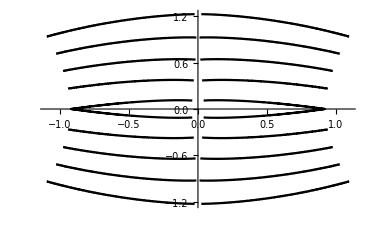

```mathematica
ListLinePlot[{PPLowerCut0,NPLowerCut0,NNLowerCut0,PNLowerCut0,
PPLowerCut200,NPLowerCut200,NNLowerCut200,PNLowerCut200,
PPLowerCut400,NPLowerCut400,NNLowerCut400,PNLowerCut400,
PPLowerCut600,NPLowerCut600,NNLowerCut600,PNLowerCut600,
PPLowerCut800,NPLowerCut800,NNLowerCut800,PNLowerCut800},PlotStyle->Black]
```

### Last Boundary in 2D

```mathematica
PPLastBoundary200=CSLastBoundary2D[{0.9239453620743007,0},{0,894},{200,923},{179},1];
NPLastBoundary200=Table[{-1,1},{i,1,179}]*PPLastBoundary200;
NNLastBoundary200=Table[{-1,-1},{i,1,179}]*PPLastBoundary200;
PNLastBoundary200=Table[{1,-1},{i,1,179}]*PPLastBoundary200;
```

```mathematica
PPLastBoundary400=CSLastBoundary2D[{0.9239453620743007,0},{200,923},{400,975},{180},1];
NPLastBoundary400=Table[{-1,1},{i,1,180}]*PPLastBoundary400;
NNLastBoundary400=Table[{-1,-1},{i,1,180}]*PPLastBoundary400;
PNLastBoundary400=Table[{1,-1},{i,1,180}]*PPLastBoundary400;
```

```mathematica
PPLastBoundary600=CSLastBoundary2D[{0.9239453620743007,0},{400,975},{600,1040},{179},1];
NPLastBoundary600=Table[{-1,1},{i,1,179}]*PPLastBoundary600;
NNLastBoundary600=Table[{-1,-1},{i,1,179}]*PPLastBoundary600;
PNLastBoundary600=Table[{1,-1},{i,1,179}]*PPLastBoundary600;
```

```mathematica
PPLastBoundary800=CSLastBoundary2D[{0.9239453620743007,0},{600,1040},{800,1112},{180},1];
NPLastBoundary800=Table[{-1,1},{i,1,180}]*PPLastBoundary800;
NNLastBoundary800=Table[{-1,-1},{i,1,180}]*PPLastBoundary800;
PNLastBoundary800=Table[{1,-1},{i,1,180}]*PPLastBoundary800;
```

```mathematica
PPLastBoundary1000=CSLastBoundary2D[{0.9239453620743007,0},{800,1112},{1000,1188},{180},1];
NPLastBoundary1000=Table[{-1,1},{i,1,180}]*PPLastBoundary1000;
NNLastBoundary1000=Table[{-1,-1},{i,1,180}]*PPLastBoundary1000;
PNLastBoundary1000=Table[{1,-1},{i,1,180}]*PPLastBoundary1000;
```

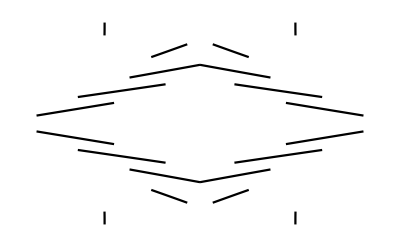

```mathematica
ListLinePlot[{PPLastBoundary200,NPLastBoundary200,NNLastBoundary200,PNLastBoundary200,
PPLastBoundary400,NPLastBoundary400,NNLastBoundary400,PNLastBoundary400,
PPLastBoundary600,NPLastBoundary600,NNLastBoundary600,PNLastBoundary600,
PPLastBoundary800,NPLastBoundary800,NNLastBoundary800,PNLastBoundary800,
PPLastBoundary1000,NPLastBoundary1000,NNLastBoundary1000,PNLastBoundary1000},PlotStyle->Black,Axes-> None]
```

## (b)

### Draw the line

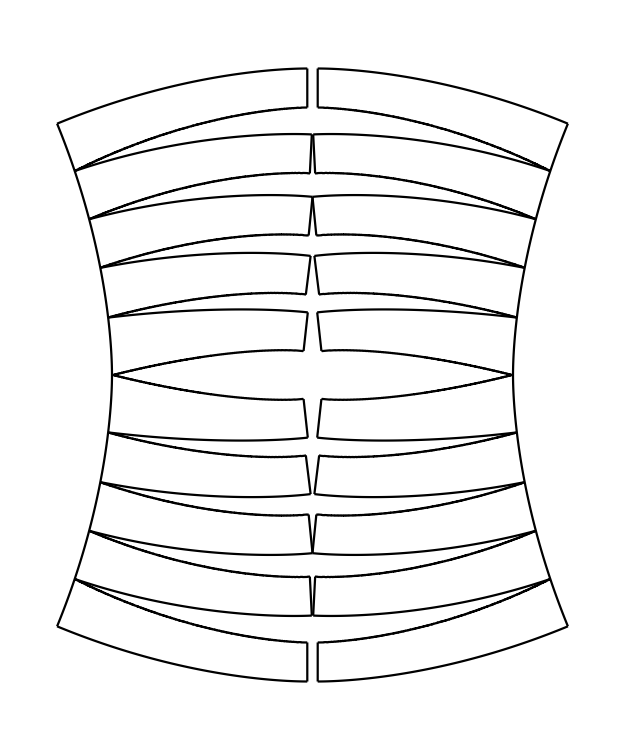

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,PlotRange-> All,AspectRatio-> 1.2,Axes-> None]
```

(c),(e)

## Set up

```mathematica
kernelcodeCS="
#define min 0
#define max 1
#define vvv 0
#define uuu 1
#define sign1 -1
#define h 0.001
#define n 1201
#define AlphaLAC (2.0)
#define BetaLASC (2.0)
#define InitRCLAC (1.0)
#define OmegaLASC (1.0)
#define Lambda_Max_LAC (12.718433357775211)
#define ArcLength_Max_LAC (6.764357890136049)
#define Lambda_Min_LAC (12.718433357775211)
#define ArcLength_Min_LAC (6.764357890136049)
#define Lambda_Max_LASC (6.285247558593747)
#define InitRT_Max_LASC (7.303131835937503)
#define ArcLength_Max_LASC (3.1084204465150833)
#define Lambda_Min_LASC (6.285247558593747)
#define InitRT_Min_LASC (7.303131835937503)
#define ArcLength_Min_LASC (3.1084204465150833)
#define Point00x (0.0)
#define Point00y (0.0)
#define Point00z (0.0)
#define Point03x (-0.7077264466498845)
#define Point03y (0.0)
#define Point03z (0.5008767232876717)
#define Point30x (0.0)
#define Point30y (-0.7077264466498845)
#define Point30z (-0.5008767232876717)
#define Point33x (-1.0013149889663)
#define Point33y (-1.0013149889663)
#define Point33z (0.0)

#define maxPoint00x (0.0)
#define maxPoint00y (0.0)
#define maxPoint00z (0.0)
#define maxPoint03x (-0.7077264466498845)
#define maxPoint03y (0.0)
#define maxPoint03z (0.5008767232876717)
#define maxPoint30x (0.0)
#define maxPoint30y (-0.7077264466498845)
#define maxPoint30z (-0.5008767232876717)
#define maxPoint33x (-1.0013149889663)
#define maxPoint33y (-1.0013149889663)
#define maxPoint33z (0.0)


#define ScaleToOrigin_Max_LAC (0.13192365851313362)
#define ScaleToOrigin_Min_LAC (0.13192365851313362)
#define ScaleToOrigin_Max_LASC (0.38164320308766897)
#define ScaleToOrigin_Min_LASC (0.38164320308766897)

#define inidxdu1 ((1-pv)*(maxPoint00x-maxPoint03x)+pv*(maxPoint30x-maxPoint33x)-v1_x1+v2_x1+(1-pv)*u1_t1+pv*u2_t1)
#define inidxdu2 ((1-pv)*(maxPoint00y-maxPoint03y)+pv*(maxPoint30y-maxPoint33y)-v1_x2+v2_x2+(1-pv)*u1_t2+pv*u2_t2)
#define inidxdu3 ((1-pv)*(maxPoint00z-maxPoint03z)+pv*(maxPoint30z-maxPoint33z)-v1_x3+v2_x3+(1-pv)*u1_t3+pv*u2_t3)
#define inidxdv1 ((1-pu)*(maxPoint00x-maxPoint30x)+pu*(maxPoint03x-maxPoint33x)-u1_x1+u2_x1+(1-pu)*v1_t1+pu*v2_t1)
#define inidxdv2 ((1-pu)*(maxPoint00y-maxPoint30y)+pu*(maxPoint03y-maxPoint33y)-u1_x2+u2_x2+(1-pu)*v1_t2+pu*v2_t2)
#define inidxdv3 ((1-pu)*(maxPoint00z-maxPoint30z)+pu*(maxPoint03z-maxPoint33z)-u1_x3+u2_x3+(1-pu)*v1_t3+pu*v2_t3)

#define inid2xdu21 ((1-pv)*u1_dt1+pv*u2_dt1)
#define inid2xdu22 ((1-pv)*u1_dt2+pv*u2_dt2)
#define inid2xdu23 ((1-pv)*u1_dt3+pv*u2_dt3)
#define inid2xdv21 ((1-pu)*v1_dt1+pu*v2_dt1)
#define inid2xdv22 ((1-pu)*v1_dt2+pu*v2_dt2)
#define inid2xdv23 ((1-pu)*v1_dt3+pu*v2_dt3)
#define inid2xdudv1 (-maxPoint00x+maxPoint03x+maxPoint30x-maxPoint33x-u1_t1+u2_t1-v1_t1+v2_t1)
#define inid2xdudv2 (-maxPoint00y+maxPoint03y+maxPoint30y-maxPoint33y-u1_t2+u2_t2-v1_t2+v2_t2)
#define inid2xdudv3 (-maxPoint00z+maxPoint03z+maxPoint30z-maxPoint33z-u1_t3+u2_t3-v1_t3+v2_t3)


#define dxdu1 ((1-pv[i])*(maxPoint00x-maxPoint03x)+pv[i]*(maxPoint30x-maxPoint33x)-v1_x1[i]+v2_x1[i]+(1-pv[i])*u1_t1[i]+pv[i]*u2_t1[i])
#define dxdu2 ((1-pv[i])*(maxPoint00y-maxPoint03y)+pv[i]*(maxPoint30y-maxPoint33y)-v1_x2[i]+v2_x2[i]+(1-pv[i])*u1_t2[i]+pv[i]*u2_t2[i])
#define dxdu3 ((1-pv[i])*(maxPoint00z-maxPoint03z)+pv[i]*(maxPoint30z-maxPoint33z)-v1_x3[i]+v2_x3[i]+(1-pv[i])*u1_t3[i]+pv[i]*u2_t3[i])
#define dxdv1 ((1-pu[i])*(maxPoint00x-maxPoint30x)+pu[i]*(maxPoint03x-maxPoint33x)-u1_x1[i]+u2_x1[i]+(1-pu[i])*v1_t1[i]+pu[i]*v2_t1[i])
#define dxdv2 ((1-pu[i])*(maxPoint00y-maxPoint30y)+pu[i]*(maxPoint03y-maxPoint33y)-u1_x2[i]+u2_x2[i]+(1-pu[i])*v1_t2[i]+pu[i]*v2_t2[i])
#define dxdv3 ((1-pu[i])*(maxPoint00z-maxPoint30z)+pu[i]*(maxPoint03z-maxPoint33z)-u1_x3[i]+u2_x3[i]+(1-pu[i])*v1_t3[i]+pu[i]*v2_t3[i])


#define d2xdu21 ((1-pv[i])*u1_dt1[i]+pv[i]*u2_dt1[i])
#define d2xdu22 ((1-pv[i])*u1_dt2[i]+pv[i]*u2_dt2[i])
#define d2xdu23 ((1-pv[i])*u1_dt3[i]+pv[i]*u2_dt3[i])
#define d2xdv21 ((1-pu[i])*v1_dt1[i]+pu[i]*v2_dt1[i])
#define d2xdv22 ((1-pu[i])*v1_dt2[i]+pu[i]*v2_dt2[i])
#define d2xdv23 ((1-pu[i])*v1_dt3[i]+pu[i]*v2_dt3[i])
#define d2xdudv1 (-maxPoint00x+maxPoint03x+maxPoint30x-maxPoint33x-u1_t1[i]+u2_t1[i]-v1_t1[i]+v2_t1[i])
#define d2xdudv2 (-maxPoint00y+maxPoint03y+maxPoint30y-maxPoint33y-u1_t2[i]+u2_t2[i]-v1_t2[i]+v2_t2[i])
#define d2xdudv3 (-maxPoint00z+maxPoint03z+maxPoint30z-maxPoint33z-u1_t3[i]+u2_t3[i]-v1_t3[i]+v2_t3[i])


#define d3xdu31 ((1-pv[i])*u1_d2t1[i]+pv[i]*u2_d2t1[i])
#define d3xdu32 ((1-pv[i])*u1_d2t2[i]+pv[i]*u2_d2t2[i])
#define d3xdu33 ((1-pv[i])*u1_d2t3[i]+pv[i]*u2_d2t3[i])
#define d3xdv31 ((1-pu[i])*v1_d2t1[i]+pu[i]*v2_d2t1[i])
#define d3xdv32 ((1-pu[i])*v1_d2t2[i]+pu[i]*v2_d2t2[i])
#define d3xdv33 ((1-pu[i])*v1_d2t3[i]+pu[i]*v2_d2t3[i])
#define d3xdu2dv1 (-u1_dt1[i]+u2_dt1[i])
#define d3xdu2dv2 (-u1_dt2[i]+u2_dt2[i])
#define d3xdu2dv3 (-u1_dt3[i]+u2_dt3[i])
#define d3xdudv21 (-v1_dt1[i]+v2_dt1[i])
#define d3xdudv22 (-v1_dt2[i]+v2_dt2[i])
#define d3xdudv23 (-v1_dt3[i]+v2_dt3[i])

#define d4xdu41 ((1-pv[i])*u1_d3t1[i]+pv[i]*u2_d3t1[i])
#define d4xdu42 ((1-pv[i])*u1_d3t2[i]+pv[i]*u2_d3t2[i])
#define d4xdu43 ((1-pv[i])*u1_d3t3[i]+pv[i]*u2_d3t3[i])
#define d4xdv41 ((1-pu[i])*v1_d3t1[i]+pu[i]*v2_d3t1[i])
#define d4xdv42 ((1-pu[i])*v1_d3t2[i]+pu[i]*v2_d3t2[i])
#define d4xdv43 ((1-pu[i])*v1_d3t3[i]+pu[i]*v2_d3t3[i])
#define d4xdu3dv1 (-u1_d2t1[i]+u2_d2t1[i])
#define d4xdu3dv2 (-u1_d2t2[i]+u2_d2t2[i])
#define d4xdu3dv3 (-u1_d2t3[i]+u2_d2t3[i])
#define d4xdudv31 (-v1_d2t1[i]+v2_d2t1[i])
#define d4xdudv32 (-v1_d2t2[i]+v2_d2t2[i])
#define d4xdudv33 (-v1_d2t3[i]+v2_d2t3[i])
#define d4xdu2dv21 (0.0)
#define d4xdu2dv22 (0.0)
#define d4xdu2dv23 (0.0)

#define Coons_x1 ((1-pv[index])*u1_x1[index]+pv[index]*u2_x1[index]+(1-pu[index])*v1_x1[index]+pu[index]*v2_x1[index]-((1-pu[index])*(1-pv[index])*maxPoint00x+pu[index]*(1-pv[index])*maxPoint03x+(1-pu[index])*pv[index]*maxPoint30x+pu[index]*pv[index]*maxPoint33x))
#define Coons_x2 ((1-pv[index])*u1_x2[index]+pv[index]*u2_x2[index]+(1-pu[index])*v1_x2[index]+pu[index]*v2_x2[index]-((1-pu[index])*(1-pv[index])*maxPoint00y+pu[index]*(1-pv[index])*maxPoint03y+(1-pu[index])*pv[index]*maxPoint30y+pu[index]*pv[index]*maxPoint33y))
#define Coons_x3 ((1-pv[index])*u1_x3[index]+pv[index]*u2_x3[index]+(1-pu[index])*v1_x3[index]+pu[index]*v2_x3[index]-((1-pu[index])*(1-pv[index])*maxPoint00z+pu[index]*(1-pv[index])*maxPoint03z+(1-pu[index])*pv[index]*maxPoint30z+pu[index]*pv[index]*maxPoint33z))

#define repiniSurNorvec iniSurNorvec(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,normv_C)
#define repinicoefE inicoefE(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repinicoefF inicoefF(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repinicoefG inicoefG(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repinicoefL inicoefL(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repinicoefM inicoefM(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repinicoefN inicoefN(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniMeanCurva iniMeanCurva(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniGaussCurva iniGaussCurva(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniMaxPrinci iniMaxPrinci(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniMinPrinci iniMinPrinci(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repiniPrinci iniPrinci(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniEta iniEta(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniMiu iniMiu(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDuDs iniDuDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repiniDvDs iniDvDs(pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)

#define repSurNorvec SurNorvec(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,normv_C)
#define repDSurNvDu DSurNvDu(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,dnormvdu_C)
#define repDSurNvDv DSurNvDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,dnormvdv_C)
#define repD2SurNvDu2 D2SurNvDu2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,d2normvdu2_C)
#define repD2SurNvDuDv D2SurNvDuDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,d2normvdudv_C)
#define repD2SurNvDv2 D2SurNvDv2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,d2normvdv2_C)
#define repScalarSurNor ScalarSurNor(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,Scal)
#define repcoefE coefE(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repDEDu DEDu(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repDEDv DEDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repD2EDu2 D2EDu2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2EDuDv D2EDuDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2EDv2 D2EDv2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repcoefF coefF(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repDFDu DFDu(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repDFDv DFDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repD2FDu2 D2FDu2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2FDuDv D2FDuDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2FDv2 D2FDv2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repcoefG coefG(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3)
#define repDGDu DGDu(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repDGDv DGDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repD2GDu2 D2GDu2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2GDuDv D2GDuDv(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repD2GDv2 D2GDv2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3)
#define repcoefL coefL(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repcoefM coefM(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repcoefN coefN(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repGaussCurva GaussCurva(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repMeanCurva MeanCurva(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repMaxPrinci MaxPrinci(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repMinPrinci MinPrinci(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3)
#define repPrinci Princi(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDcoefL_2 DcoefL_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,CoeffL)
#define repDcoefM_2 DcoefM_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,CoeffM)
#define repDcoefN_2 DcoefN_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,CoeffN)
#define repDGaussCurva_2 DGaussCurva_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,GCurva)
#define repDMeanCurva_2 DMeanCurva_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,MCurva)
#define repDPrinci_2 DPrinci_2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum,PCurva)
#define repEta Eta(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repMiu  Miu(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDuDs DuDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDuDs1 DuDs(i+1,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDvDs DvDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDvDs1 DvDs(i+1,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDEDs DEDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDFDs DFDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDGDs DGDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDLDs DLDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repDMDs DMDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repDNDs DNDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repDPrinciDs DPrinciDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repDvDt DvDt(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDuDt DuDt(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum)
#define repDSurDs DSurDs(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum,tangv)
#define repD2uDs2 D2uDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2vDs2 D2vDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repGeoCur GeoCur(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repCurvecurvature Curvecurvature(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2EDs2 D2EDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2FDs2 D2FDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2GDs2 D2GDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2LDs2 D2LDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2MDs2 D2MDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2NDs2 D2NDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2PrinciDs2 D2PrinciDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)
#define repD2SurDs2 D2SurDs2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum,dtangds)
#define repCurvenormaloS CurvenormaloS(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum,norv)
#define repCurvebinormaloS CurvebinormaloS(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum,binorv)
#define repAlp2 Alp2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum,Alp2_C)
#define repBeta2 Beta2(i,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum)


#define opt1 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float normv_C[])
#define opt2 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3)
#define opt3 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3)
#define opt4 (float pu,float pv,float u1_x1,float u1_x2,float u1_x3,float u1_t1,float u1_t2,float u1_t3,float u1_dt1,float u1_dt2,float u1_dt3,float u2_x1,float u2_x2,float u2_x3,float u2_t1,float u2_t2,float u2_t3,float u2_dt1,float u2_dt2,float u2_dt3,float v1_x1,float v1_x2,float v1_x3,float v1_t1,float v1_t2,float v1_t3,float v1_dt1,float v1_dt2,float v1_dt3,float v2_x1,float v2_x2,float v2_x3,float v2_t1,float v2_t2,float v2_t3,float v2_dt1,float v2_dt2,float v2_dt3,mint optimum)
#define opt5 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float normv_C[]) 
#define opt6 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[])
#define opt7 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[])
#define opt8 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],mint optimum)
#define opt9 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],mint optimum,float tangv_C[])
#define opt10 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float dnormv_C[])
#define opt11 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float d2normv_C[])
#define opt12 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float Scal[])
#define opt13 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[])
#define opt14 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u1_d3t1[],float u1_d3t2[],float u1_d3t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float u2_d3t1[],float u2_d3t2[],float u2_d3t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v1_d3t1[],float v1_d3t2[],float v1_d3t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float v2_d3t1[],float v2_d3t2[],float v2_d3t3[],float coeff[])
#define opt15 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u1_d3t1[],float u1_d3t2[],float u1_d3t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float u2_d3t1[],float u2_d3t2[],float u2_d3t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v1_d3t1[],float v1_d3t2[],float v1_d3t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float v2_d3t1[],float v2_d3t2[],float v2_d3t3[],mint optimum,float coeff[])
#define opt16 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u1_d2t1[],float u1_d2t2[],float u1_d2t3[],float u1_d3t1[],float u1_d3t2[],float u1_d3t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float u2_d2t1[],float u2_d2t2[],float u2_d2t3[],float u2_d3t1[],float u2_d3t2[],float u2_d3t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v1_d2t1[],float v1_d2t2[],float v1_d2t3[],float v1_d3t1[],float v1_d3t2[],float v1_d3t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],float v2_d2t1[],float v2_d2t2[],float v2_d2t3[],float v2_d3t1[],float v2_d3t2[],float v2_d3t3[],mint optimum)
#define opt17 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],mint optimum,float Alph_C[])
#define opt18 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float Snor_C[])
#define opt19 (int i,float pu[],float pv[],float u1_x1[],float u1_x2[],float u1_x3[],float u1_t1[],float u1_t2[],float u1_t3[],float u1_dt1[],float u1_dt2[],float u1_dt3[],float u2_x1[],float u2_x2[],float u2_x3[],float u2_t1[],float u2_t2[],float u2_t3[],float u2_dt1[],float u2_dt2[],float u2_dt3[],float v1_x1[],float v1_x2[],float v1_x3[],float v1_t1[],float v1_t2[],float v1_t3[],float v1_dt1[],float v1_dt2[],float v1_dt3[],float v2_x1[],float v2_x2[],float v2_x3[],float v2_t1[],float v2_t2[],float v2_t3[],float v2_dt1[],float v2_dt2[],float v2_dt3[],mint optimum,float binormv_C[])

__device__ float inicurvature_LAC(float t,float Alpha,float Lambda,float InitRC,float Total_s) 
{
if(Alpha==-1)
	{return ((float) 1)/InitRC-Lambda*t*Total_s;}
else if(Alpha==0) 
	{return ((float) 1)/exp(Lambda*t*Total_s+log(InitRC));} 
else if(Alpha==1)
	{return ((float) 1)/(InitRC+Lambda*t*Total_s);}
else if(Alpha==2)
	{return ((float) 1)/sqrt(pow(InitRC,2)+((float) 2)*Lambda*t*Total_s);}
else
	{return pow(pow(InitRC,Alpha)+Lambda*Alpha*t*Total_s,-((float) 1)/Alpha);}
}

__device__ float inidcLACdx(float t,float Alpha,float Lambda,float InitRC,float Total_s) 
{
if(Alpha==-1)
	{return -Total_s*Lambda;}
else if(Alpha==0) 
	{return -Total_s*(Lambda*exp(-Lambda*t*Total_s))/InitRC;} 
else if(Alpha==1)
	{return -Total_s*Lambda/pow(InitRC+Lambda*t*Total_s,2);}
else if(Alpha==2)
	{return -Total_s*Lambda/sqrt(pow(pow(InitRC,2)+((float) 2)*Lambda*t*Total_s,3));}
else
	{return -Total_s*Lambda*pow(pow(InitRC,Alpha)+Lambda*Alpha*t*Total_s,-((float) 1)-((float) 1)/Alpha);}
}
__device__ float inid2cLACdx2(float t,float Alpha,float Lambda,float InitRC,float Total_s) 
{
if(Alpha==-1)
	{return 0;}
else if(Alpha==0) 
	{return pow(Total_s,2)*(pow(Lambda,2)*exp(-Lambda*t*Total_s))/InitRC;} 
else if(Alpha==1)
	{return pow(Total_s,2)*((float) 2)*pow(Lambda,2)/pow(InitRC+Lambda*t*Total_s,3);}
else if(Alpha==2)
	{return pow(Total_s,2)*(((float) 3)*pow(Lambda,2))/sqrt(pow(pow(InitRC,2)+((float) 2)*Lambda*t*Total_s,5));}
else
	{return (((float) 1)+Alpha)*pow(Total_s,2)*pow(Lambda,2)*pow(pow(InitRC,Alpha)+Lambda*Alpha*t*Total_s,-((float) 2)-((float) 1)/Alpha);}
}

__device__ float iniTorsion_LAC(float t,float Beta,float Omega,float InitRT,float Total_s) 
{
if(Beta==-1)
	{return ((float) 1)/InitRT-Omega*t*Total_s;}
else if(Beta==0) 
	{return ((float) 1)/exp(Omega*t*Total_s+log(InitRT));} 
else if(Beta==1)
	{return ((float) 1)/(InitRT+Omega*t*Total_s);}
else if(Beta==2)
	{return ((float) 1)/sqrt(pow(InitRT,2)+((float) 2)*Omega*t*Total_s);}
else
	{return pow(pow(InitRT,Beta)+Omega*Beta*t*Total_s,-((float) 1)/Beta);}
}

__device__ float inidtLACdx(float t,float Beta,float Omega,float InitRT,float Total_s) 
{
if(Beta==-1)
	{return -Total_s*Omega;}
else if(Beta==0) 
	{return -Total_s*(Omega*exp(-Omega*t*Total_s))/InitRT;} 
else if(Beta==1)
	{return -Total_s*Omega/pow(InitRT+Omega*t*Total_s,2);}
else if(Beta==2)
	{return -Total_s*Omega/sqrt(pow(pow(InitRT,2)+((float) 2)*Omega*t*Total_s,3));}
else
	{return -Total_s*Omega*pow(pow(InitRT,Beta)+Omega*Beta*t*Total_s,-((float) 1)-((float) 1)/Beta);}
}


__device__ void iniSurNorvec opt1 
{
	normv_C[0] =inidxdu2*inidxdv3-inidxdu3*inidxdv2; 
	normv_C[1] =inidxdu3*inidxdv1-inidxdu1*inidxdv3;
	normv_C[2] =inidxdu1*inidxdv2-inidxdu2*inidxdv1; 
}
__device__ float inicoefE opt2 
{
	return inidxdu1*inidxdu1+inidxdu2*inidxdu2+inidxdu3*inidxdu3; 
}
__device__ float inicoefF opt2 
{ 
	return (inidxdu1*inidxdv1+inidxdu2*inidxdv2+inidxdu3*inidxdv3); 
}

__device__ float inicoefG opt2 
{ 
	return inidxdv1*inidxdv1+inidxdv2*inidxdv2+inidxdv3*inidxdv3; 
}
__device__ float inicoefL opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdu21+normv_C[1]*inid2xdu22+normv_C[2]*inid2xdu23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float inicoefM opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdudv1+normv_C[1]*inid2xdudv2+normv_C[2]*inid2xdudv3)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float inicoefN opt3
{
float normv_C[3];
repiniSurNorvec;

	return (normv_C[0]*inid2xdv21+normv_C[1]*inid2xdv22+normv_C[2]*inid2xdv23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float iniGaussCurva opt3
{
	return (repinicoefL*repinicoefN-pow(repinicoefM,2))/(repinicoefE*repinicoefG-pow(repinicoefF,2)); 
}
__device__ float iniMeanCurva opt3
{
	return 0.5*(repinicoefE*repinicoefN+repinicoefG*repinicoefL-2*repinicoefF*repinicoefM)/(repinicoefE*repinicoefG-pow(repinicoefF,2));
}
__device__ float iniMaxPrinci opt3
{
	return repiniMeanCurva+sqrt(pow(repiniMeanCurva,2)-repiniGaussCurva); 
}

__device__ float iniMinPrinci opt3
{
	return repiniMeanCurva-sqrt(pow(repiniMeanCurva,2)-repiniGaussCurva); 
}
__device__ float iniPrinci opt4
{ 	
	if(optimum==max) 
	{return repiniMaxPrinci;} 
	else if(optimum==min)
	{return repiniMinPrinci;}
	else
	{return 0;}
}
__device__ float iniEta opt4
{
	return sign1/sqrt(repinicoefE*pow(repinicoefM-repiniPrinci*repinicoefF,2)-2*repinicoefF*(repinicoefM-repiniPrinci*repinicoefF)*(repinicoefL-repiniPrinci*repinicoefE)+repinicoefG*pow(repinicoefL-repiniPrinci*repinicoefE,2));
}
__device__ float iniMiu opt4
{
	return sign1/sqrt(repinicoefE*pow(repinicoefN-repiniPrinci*repinicoefG,2)-2*repinicoefF*(repinicoefM-repiniPrinci*repinicoefF)*(repinicoefN-repiniPrinci*repinicoefG)+repinicoefG*pow(repinicoefM-repiniPrinci*repinicoefF,2));
}

__device__ float iniDuDs opt4
{ 
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return repiniEta*(repinicoefM-repiniPrinci*repinicoefF);}
else
	{return repiniMiu*(repinicoefN-repiniPrinci*repinicoefG);}
}
__device__ float iniDvDs opt4
{
if(abs(repinicoefL-repiniPrinci*repinicoefE)>=abs(repinicoefN-repiniPrinci*repinicoefG))
	{return -repiniEta*(repinicoefL-repiniPrinci*repinicoefE);}
else
	{return -repiniMiu*(repinicoefM-repiniPrinci*repinicoefF);}
}

__device__ void SurNorvec opt5 
{
	normv_C[0] =dxdu2*dxdv3-dxdu3*dxdv2; 
	normv_C[1] =dxdu3*dxdv1-dxdu1*dxdv3;
	normv_C[2] =dxdu1*dxdv2-dxdu2*dxdv1; 
}
__device__ void DSurNvDu opt10
{
	dnormv_C[0] =(d2xdu22*dxdv3-d2xdu23*dxdv2)+(dxdu2*d2xdudv3-dxdu3*d2xdudv2); 
	dnormv_C[1] =(d2xdu23*dxdv1-d2xdu21*dxdv3)+(dxdu3*d2xdudv1-dxdu1*d2xdudv3);
	dnormv_C[2] =(d2xdu21*dxdv2-d2xdu22*dxdv1)+(dxdu1*d2xdudv2-dxdu2*d2xdudv1); 
}
__device__ void DSurNvDv opt10
{
	dnormv_C[0] =(d2xdudv2*dxdv3-d2xdudv3*dxdv2)+(dxdu2*d2xdv23-dxdu3*d2xdv22); 
	dnormv_C[1] =(d2xdudv3*dxdv1-d2xdudv1*dxdv3)+(dxdu3*d2xdv21-dxdu1*d2xdv23); 
	dnormv_C[2] =(d2xdudv1*dxdv2-d2xdudv2*dxdv1)+(dxdu1*d2xdv22-dxdu2*d2xdv21); 
}
__device__ void D2SurNvDu2 opt11
{
	d2normv_C[0] =(d3xdu32*dxdv3-d3xdu33*dxdv2)+2*(d2xdu22*d2xdudv3-d2xdu23*d2xdudv2)+(dxdu2*d3xdu2dv3-dxdu3*d3xdu2dv2); 
	d2normv_C[1] =(d3xdu33*dxdv1-d3xdu31*dxdv3)+2*(d2xdu23*d2xdudv1-d2xdu21*d2xdudv3)+(dxdu3*d3xdu2dv1-dxdu1*d3xdu2dv3); 
	d2normv_C[2] =(d3xdu31*dxdv2-d3xdu32*dxdv1)+2*(d2xdu21*d2xdudv2-d2xdu22*d2xdudv1)+(dxdu1*d3xdu2dv2-dxdu2*d3xdu2dv1); 
}
__device__ void D2SurNvDuDv opt11
{
	d2normv_C[0] =(d3xdu2dv2*dxdv3-d3xdu2dv3*dxdv2)+(d2xdu22*d2xdv23-d2xdu23*d2xdv22)+(dxdu2*d3xdudv23-dxdu3*d3xdudv22); 
	d2normv_C[1] =(d3xdu2dv3*dxdv1-d3xdu2dv1*dxdv3)+(d2xdu23*d2xdv21-d2xdu21*d2xdv23)+(dxdu3*d3xdudv21-dxdu1*d3xdudv23); 
	d2normv_C[2] =(d3xdu2dv1*dxdv2-d3xdu2dv2*dxdv1)+(d2xdu21*d2xdv22-d2xdu22*d2xdv21)+(dxdu1*d3xdudv22-dxdu2*d3xdudv21); 
}
__device__ void D2SurNvDv2 opt11
{
	d2normv_C[0] =(d3xdudv22*dxdv3-d3xdudv23*dxdv2)+2*(d2xdudv2*d2xdv23-d2xdudv3*d2xdv22)+(dxdu2*d3xdv33-dxdu3*d3xdv32); 
	d2normv_C[1] =(d3xdudv23*dxdv1-d3xdudv21*dxdv3)+2*(d2xdudv3*d2xdv21-d2xdudv1*d2xdv23)+(dxdu3*d3xdv31-dxdu1*d3xdv33); 
	d2normv_C[2] =(d3xdudv21*dxdv2-d3xdudv22*dxdv1)+2*(d2xdudv1*d2xdv22-d2xdudv2*d2xdv21)+(dxdu1*d3xdv32-dxdu2*d3xdv31); 
}
__device__ void ScalarSurNor opt12
{
float ScalSNor,DScalSNorDu,DScalSNorDv,D2ScalSNorDu2,D2ScalSNorDuDv,D2ScalSNorDv2;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float d2normvdu2_C[3];
float d2normvdudv_C[3];
float d2normvdv2_C[3];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repD2SurNvDu2;
repD2SurNvDuDv;
repD2SurNvDv2;

ScalSNor = sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
DScalSNorDu = (normv_C[0]*dnormvdu_C[0]+normv_C[1]*dnormvdu_C[1]+normv_C[2]*dnormvdu_C[2])/ScalSNor;
DScalSNorDv = (normv_C[0]*dnormvdv_C[0]+normv_C[1]*dnormvdv_C[1]+normv_C[2]*dnormvdv_C[2])/ScalSNor;
D2ScalSNorDu2 = ((normv_C[0]*d2normvdu2_C[0]+normv_C[1]*d2normvdu2_C[1]+normv_C[2]*d2normvdu2_C[2])+(dnormvdu_C[0]*dnormvdu_C[0]+dnormvdu_C[1]*dnormvdu_C[1]+dnormvdu_C[2]*dnormvdu_C[2])-pow(DScalSNorDu,2))/ScalSNor;
D2ScalSNorDuDv = ((normv_C[0]*d2normvdudv_C[0]+normv_C[1]*d2normvdudv_C[1]+normv_C[2]*d2normvdudv_C[2])+(dnormvdu_C[0]*dnormvdv_C[0]+dnormvdu_C[1]*dnormvdv_C[1]+dnormvdu_C[2]*dnormvdv_C[2])-DScalSNorDu*DScalSNorDv)/ScalSNor;
D2ScalSNorDv2 = ((normv_C[0]*d2normvdv2_C[0]+normv_C[1]*d2normvdv2_C[1]+normv_C[2]*d2normvdv2_C[2])+(dnormvdv_C[0]*dnormvdv_C[0]+dnormvdv_C[1]*dnormvdv_C[1]+dnormvdv_C[2]*dnormvdv_C[2])-pow(DScalSNorDv,2))/ScalSNor;

Scal[0] = ScalSNor;
Scal[1] = DScalSNorDu;
Scal[2] = DScalSNorDv;
Scal[3] = D2ScalSNorDu2;
Scal[4] = D2ScalSNorDuDv;
Scal[5] = D2ScalSNorDv2;
}

__device__ float coefE opt6
{
	return dxdu1*dxdu1+dxdu2*dxdu2+dxdu3*dxdu3; 
}
__device__ float DEDu opt7
{
	return 2*(dxdu1*d2xdu21+dxdu2*d2xdu22+dxdu3*d2xdu23);
}
__device__ float DEDv opt7
{
	return 2*(dxdu1*d2xdudv1+dxdu2*d2xdudv2+dxdu3*d2xdudv3);
}
__device__ float D2EDu2 opt13
{
	return 2*((d2xdu21*d2xdu21+d2xdu22*d2xdu22+d2xdu23*d2xdu23)+(dxdu1*d3xdu31+dxdu2*d3xdu32+dxdu3*d3xdu33));
}
__device__ float D2EDuDv opt13
{
	return 2*((d2xdudv1*d2xdu21+d2xdudv2*d2xdu22+d2xdudv3*d2xdu23)+(dxdu1*d3xdu2dv1+dxdu2*d3xdu2dv2+dxdu3*d3xdu2dv3));
}
__device__ float D2EDv2 opt13
{
	return 2*((d2xdudv1*d2xdudv1+d2xdudv2*d2xdudv2+d2xdudv3*d2xdudv3)+(dxdu1*d3xdudv21+dxdu2*d3xdudv22+dxdu3*d3xdudv23));
}
 
__device__ float coefF opt6
{ 
	return (dxdu1*dxdv1+dxdu2*dxdv2+dxdu3*dxdv3); 
}
__device__ float DFDu opt7
{ 
	return dxdv1*d2xdu21+dxdv2*d2xdu22+dxdv3*d2xdu23 + dxdu1*d2xdudv1+dxdu2*d2xdudv2+dxdu3*d2xdudv3;
}
__device__ float DFDv opt7
{ 
	return dxdv1*d2xdudv1+dxdv2*d2xdudv2+dxdv3*d2xdudv3 + dxdu1*d2xdv21+dxdu2*d2xdv22+dxdu3*d2xdv23;
}
__device__ float D2FDu2 opt13
{ 
	return (dxdv1*d3xdu31+dxdv2*d3xdu32+dxdv3*d3xdu33)+2*(d2xdu21*d2xdudv1+d2xdu22*d2xdudv2+d2xdu23*d2xdudv3)+(dxdu1*d3xdu2dv1+dxdu2*d3xdu2dv2+dxdu3*d3xdu2dv3);
}
__device__ float D2FDuDv opt13
{
	return (dxdv1*d3xdu2dv1+dxdv2*d3xdu2dv2+dxdv3*d3xdu2dv3)+(d2xdu21*d2xdv21+d2xdu22*d2xdv22+d2xdu23*d2xdv23)+(d2xdudv1*d2xdudv1+d2xdudv2*d2xdudv2+d2xdudv3*d2xdudv3)+(dxdu1*d3xdudv21+dxdu2*d3xdudv22+dxdu3*d3xdudv23);
}
__device__ float D2FDv2 opt13
{
	return (dxdv1*d3xdudv21+dxdv2*d3xdudv22+dxdv3*d3xdudv23)+2*(d2xdudv1*d2xdv21+d2xdudv2*d2xdv22+d2xdudv3*d2xdv23)+(dxdu1*d3xdv31+dxdu2*d3xdv32+dxdu3*d3xdv33);
}
__device__ float coefG opt6
{ 
	return dxdv1*dxdv1+dxdv2*dxdv2+dxdv3*dxdv3; 
}
__device__ float DGDu opt7
{ 
	return 2*(dxdv1*d2xdudv1+dxdv2*d2xdudv2+dxdv3*d2xdudv3);
}
__device__ float DGDv opt7
{ 
	return 2*(dxdv1*d2xdv21+dxdv2*d2xdv22+dxdv3*d2xdv23);
}
__device__ float D2GDu2 opt13
{ 
	return 2*((d2xdudv1*d2xdudv1+d2xdudv2*d2xdudv2+d2xdudv3*d2xdudv3)+(dxdv1*d3xdu2dv1+dxdv2*d3xdu2dv2+dxdv3*d3xdu2dv3));
}
__device__ float D2GDuDv opt13
{ 
	return 2*((d2xdv21*d2xdudv1+d2xdv22*d2xdudv2+d2xdv23*d2xdudv3)+(dxdv1*d3xdudv21+dxdv2*d3xdudv22+dxdv3*d3xdudv23));
}
__device__ float D2GDv2 opt13
{ 
	return 2*((d2xdv21*d2xdv21+d2xdv22*d2xdv22+d2xdv23*d2xdv23)+(dxdv1*d3xdv31+dxdv2*d3xdv32+dxdv3*d3xdv33));
}
__device__ float coefL opt7
{
float normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdu21+normv_C[1]*d2xdu22+normv_C[2]*d2xdu23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float coefM opt7
{
float normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdudv1+normv_C[1]*d2xdudv2+normv_C[2]*d2xdudv3)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float coefN opt7
{
float normv_C[3];
repSurNorvec;

	return (normv_C[0]*d2xdv21+normv_C[1]*d2xdv22+normv_C[2]*d2xdv23)/sqrt(normv_C[0]*normv_C[0]+normv_C[1]*normv_C[1]+normv_C[2]*normv_C[2]);
}
__device__ float GaussCurva opt7
{
	return (repcoefL*repcoefN-pow(repcoefM,2))/(repcoefE*repcoefG-pow(repcoefF,2)); 
}
__device__ float MeanCurva opt7
{
	return 0.5*(repcoefE*repcoefN+repcoefG*repcoefL-2*repcoefF*repcoefM)/(repcoefE*repcoefG-pow(repcoefF,2));
}
__device__ float MaxPrinci opt7
{
	return repMeanCurva+sqrt(pow(repMeanCurva,2)-repGaussCurva); 
}

__device__ float MinPrinci opt7
{
	return repMeanCurva-sqrt(pow(repMeanCurva,2)-repGaussCurva); 
}
__device__ float Princi opt8
{ 	
	if(optimum==max) 
	{return repMaxPrinci;} 
	else if(optimum==min)
	{return repMinPrinci;}
	else
	{return 0;}
}
__device__ void DcoefL_2 opt14
{
float CoeL,DCoeLDu,DCoeLDv,D2CoeLDu2,D2CoeLDuDv,D2CoeLDv2;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float d2normvdu2_C[3];
float d2normvdudv_C[3];
float d2normvdv2_C[3];
float Scal[6];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repD2SurNvDu2;
repD2SurNvDuDv;
repD2SurNvDv2;
repScalarSurNor;

CoeL = (normv_C[0]*d2xdu21+normv_C[1]*d2xdu22+normv_C[2]*d2xdu23)/Scal[0];
DCoeLDu = ((dnormvdu_C[0]*d2xdu21+dnormvdu_C[1]*d2xdu22+dnormvdu_C[2]*d2xdu23)+(normv_C[0]*d3xdu31+normv_C[1]*d3xdu32+normv_C[2]*d3xdu33)-Scal[1]*CoeL)/Scal[0];
DCoeLDv = ((dnormvdv_C[0]*d2xdu21+dnormvdv_C[1]*d2xdu22+dnormvdv_C[2]*d2xdu23)+(normv_C[0]*d3xdu2dv1+normv_C[1]*d3xdu2dv2+normv_C[2]*d3xdu2dv3)-Scal[2]*CoeL)/Scal[0];
D2CoeLDu2 = ((d2normvdu2_C[0]*d2xdu21+d2normvdu2_C[1]*d2xdu22+d2normvdu2_C[2]*d2xdu23)+2*(dnormvdu_C[0]*d3xdu31+dnormvdu_C[1]*d3xdu32+dnormvdu_C[2]*d3xdu33)+(normv_C[0]*d4xdu41+normv_C[1]*d4xdu42+normv_C[2]*d4xdu43)-Scal[3]*CoeL-2*Scal[1]*DCoeLDu)/Scal[0];
D2CoeLDuDv = ((d2normvdudv_C[0]*d2xdu21+d2normvdudv_C[1]*d2xdu22+d2normvdudv_C[2]*d2xdu23)+(dnormvdu_C[0]*d3xdu2dv1+dnormvdu_C[1]*d3xdu2dv2+dnormvdu_C[2]*d3xdu2dv3)+(dnormvdv_C[0]*d3xdu31+dnormvdv_C[1]*d3xdu32+dnormvdv_C[2]*d3xdu33)+(normv_C[0]*d4xdu3dv1+normv_C[1]*d4xdu3dv2+normv_C[2]*d4xdu3dv3)-Scal[4]*CoeL-Scal[1]*DCoeLDv-Scal[2]*DCoeLDu)/Scal[0];
D2CoeLDv2 = ((d2normvdv2_C[0]*d2xdu21+d2normvdv2_C[1]*d2xdu22+d2normvdv2_C[2]*d2xdu23)+2*(dnormvdv_C[0]*d3xdu2dv1+dnormvdv_C[1]*d3xdu2dv2+dnormvdv_C[2]*d3xdu2dv3)+(normv_C[0]*d4xdu2dv21+normv_C[1]*d4xdu2dv22+normv_C[2]*d4xdu2dv23)-Scal[5]*CoeL-2*Scal[2]*DCoeLDv)/Scal[0];

coeff[0] = CoeL;
coeff[1] = DCoeLDu;
coeff[2] = DCoeLDv;
coeff[3] = D2CoeLDu2;
coeff[4] = D2CoeLDuDv;
coeff[5] = D2CoeLDv2;
}
__device__ void DcoefM_2 opt14
{
float CoeM,DCoeMDu,DCoeMDv,D2CoeMDu2,D2CoeMDuDv,D2CoeMDv2;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float d2normvdu2_C[3];
float d2normvdudv_C[3];
float d2normvdv2_C[3];
float Scal[6];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repD2SurNvDu2;
repD2SurNvDuDv;
repD2SurNvDv2;
repScalarSurNor;

CoeM = (normv_C[0]*d2xdudv1+normv_C[1]*d2xdudv2+normv_C[2]*d2xdudv3)/Scal[0];
DCoeMDu = ((dnormvdu_C[0]*d2xdudv1+dnormvdu_C[1]*d2xdudv2+dnormvdu_C[2]*d2xdudv3)+(normv_C[0]*d3xdu2dv1+normv_C[1]*d3xdu2dv2+normv_C[2]*d3xdu2dv3)-Scal[1]*CoeM)/Scal[0];
DCoeMDv = ((dnormvdv_C[0]*d2xdudv1+dnormvdv_C[1]*d2xdudv2+dnormvdv_C[2]*d2xdudv3)+(normv_C[0]*d3xdudv21+normv_C[1]*d3xdudv22+normv_C[2]*d3xdudv23)-Scal[2]*CoeM)/Scal[0];
D2CoeMDu2 = ((d2normvdu2_C[0]*d2xdudv1+d2normvdu2_C[1]*d2xdudv2+d2normvdu2_C[2]*d2xdudv3)+2*(dnormvdu_C[0]*d3xdu2dv1+dnormvdu_C[1]*d3xdu2dv2+dnormvdu_C[2]*d3xdu2dv3)+(normv_C[0]*d4xdu3dv1+normv_C[1]*d4xdu3dv2+normv_C[2]*d4xdu3dv3)-Scal[3]*CoeM-2*Scal[1]*DCoeMDu)/Scal[0];
D2CoeMDuDv = ((d2normvdudv_C[0]*d2xdudv1+d2normvdudv_C[1]*d2xdudv2+d2normvdudv_C[2]*d2xdudv3)+(dnormvdu_C[0]*d3xdudv21+dnormvdu_C[1]*d3xdudv22+dnormvdu_C[2]*d3xdudv23)+(dnormvdv_C[0]*d3xdu2dv1+dnormvdv_C[1]*d3xdu2dv2+dnormvdv_C[2]*d3xdu2dv3)+(normv_C[0]*d4xdu2dv21+normv_C[1]*d4xdu2dv22+normv_C[2]*d4xdu2dv23)-Scal[4]*CoeM-Scal[1]*DCoeMDv-Scal[2]*DCoeMDu)/Scal[0];
D2CoeMDv2 = ((d2normvdv2_C[0]*d2xdudv1+d2normvdv2_C[1]*d2xdudv2+d2normvdv2_C[2]*d2xdudv3)+2*(dnormvdv_C[0]*d3xdudv21+dnormvdv_C[1]*d3xdudv22+dnormvdv_C[2]*d3xdudv23)+(normv_C[0]*d4xdudv31+normv_C[1]*d4xdudv32+normv_C[2]*d4xdudv33)-Scal[5]*CoeM-2*Scal[2]*DCoeMDv)/Scal[0];

coeff[0] = CoeM;
coeff[1] = DCoeMDu;
coeff[2] = DCoeMDv;
coeff[3] = D2CoeMDu2;
coeff[4] = D2CoeMDuDv;
coeff[5] = D2CoeMDv2;
}
__device__ void DcoefN_2 opt14
{
float CoeN,DCoeNDu,DCoeNDv,D2CoeNDu2,D2CoeNDuDv,D2CoeNDv2;
float normv_C[3];
float dnormvdu_C[3];
float dnormvdv_C[3];
float d2normvdu2_C[3];
float d2normvdudv_C[3];
float d2normvdv2_C[3];
float Scal[6];
repSurNorvec;
repDSurNvDu;
repDSurNvDv;
repD2SurNvDu2;
repD2SurNvDuDv;
repD2SurNvDv2;
repScalarSurNor;

CoeN = (normv_C[0]*d2xdv21+normv_C[1]*d2xdv22+normv_C[2]*d2xdv23)/Scal[0];
DCoeNDu = ((dnormvdu_C[0]*d2xdv21+dnormvdu_C[1]*d2xdv22+dnormvdu_C[2]*d2xdv23)+(normv_C[0]*d3xdudv21+normv_C[1]*d3xdudv22+normv_C[2]*d3xdudv23)-Scal[1]*CoeN)/Scal[0];
DCoeNDv = ((dnormvdv_C[0]*d2xdv21+dnormvdv_C[1]*d2xdv22+dnormvdv_C[2]*d2xdv23)+(normv_C[0]*d3xdv31+normv_C[1]*d3xdv32+normv_C[2]*d3xdv33)-Scal[2]*CoeN)/Scal[0];
D2CoeNDu2 = ((d2normvdu2_C[0]*d2xdv21+d2normvdu2_C[1]*d2xdv22+d2normvdu2_C[2]*d2xdv23)+2*(dnormvdu_C[0]*d3xdudv21+dnormvdu_C[1]*d3xdudv22+dnormvdu_C[2]*d3xdudv23)+(normv_C[0]*d4xdu2dv21+normv_C[1]*d4xdu2dv22+normv_C[2]*d4xdu2dv23)-Scal[3]*CoeN-2*Scal[1]*DCoeNDu)/Scal[0];
D2CoeNDuDv = ((d2normvdudv_C[0]*d2xdv21+d2normvdudv_C[1]*d2xdv22+d2normvdudv_C[2]*d2xdv23)+(dnormvdu_C[0]*d3xdv31+dnormvdu_C[1]*d3xdv32+dnormvdu_C[2]*d3xdv33)+(dnormvdv_C[0]*d3xdudv21+dnormvdv_C[1]*d3xdudv22+dnormvdv_C[2]*d3xdudv23)+(normv_C[0]*d4xdudv31+normv_C[1]*d4xdudv32+normv_C[2]*d4xdudv33)-Scal[4]*CoeN-Scal[1]*DCoeNDv-Scal[2]*DCoeNDu)/Scal[0];
D2CoeNDv2 = ((d2normvdv2_C[0]*d2xdv21+d2normvdv2_C[1]*d2xdv22+d2normvdv2_C[2]*d2xdv23)+2*(dnormvdv_C[0]*d3xdv31+dnormvdv_C[1]*d3xdv32+dnormvdv_C[2]*d3xdv33)+(normv_C[0]*d4xdv41+normv_C[1]*d4xdv42+normv_C[2]*d4xdv43)-Scal[5]*CoeN-2*Scal[2]*DCoeNDv)/Scal[0];

coeff[0] = CoeN;
coeff[1] = DCoeNDu;
coeff[2] = DCoeNDv;
coeff[3] = D2CoeNDu2;
coeff[4] = D2CoeNDuDv;
coeff[5] = D2CoeNDv2;
}
__device__ void DGaussCurva_2 opt14 
{
float GCurv,DGCurvDu,DGCurvDv,D2GCurvDu2,D2GCurvDuDv,D2GCurvDv2;
float CoeffL[6];
float CoeffM[6];
float CoeffN[6];
repDcoefL_2;
repDcoefM_2;
repDcoefN_2;

GCurv= (CoeffL[0]*CoeffN[0]-pow(CoeffM[0],2))/(repcoefE*repcoefG-pow(repcoefF,2));
DGCurvDu = ((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*CoeffL[1]-2*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
DGCurvDv =((pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*CoeffL[2]-2*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
D2GCurvDu2 = ((-2*(pow(repcoefF,2)-repcoefE*repcoefG)*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)*(CoeffN[0]*CoeffL[1]-2*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1])+(pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(2*pow(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu,2)-(pow(repcoefF,2)-repcoefE*repcoefG)*(2*pow(repDFDu,2)-2*repDEDu*repDGDu-repcoefG*repD2EDu2+2*repcoefF*repD2FDu2-repcoefE*repD2GDu2))+pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(2*pow(CoeffM[1],2)-2*CoeffL[1]*CoeffN[1]-CoeffN[0]*CoeffL[3]+2*CoeffM[0]*CoeffM[3]-CoeffL[0]*CoeffN[3]))/pow(pow(repcoefF,2)-repcoefE*repcoefG,3));
D2GCurvDuDv = -((2*(pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*CoeffL[2]-2*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2])*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(CoeffN[0]*CoeffL[1]-2*CoeffM[0]*CoeffM[1]+CoeffL[0]*CoeffN[1])+(-pow(repcoefF,2)+repcoefE*repcoefG)*(-pow(CoeffM[0],2)+CoeffL[0]*CoeffN[0])*(repDGDv*repDEDu-2*repDFDv*repDFDu+repDEDv*repDGDu+repcoefG*repD2EDuDv-2*repcoefF*repD2FDuDv+repcoefE*repD2GDuDv)-pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(CoeffN[2]*CoeffL[1]-2*CoeffM[2]*CoeffM[1]+CoeffL[2]*CoeffN[1]+CoeffN[0]*CoeffL[4]-2*CoeffM[0]*CoeffM[4]+CoeffL[0]*CoeffN[4]))/pow(-pow(repcoefF,2)+repcoefE*repcoefG,3));
D2GCurvDv2 = ((-2*(pow(repcoefF,2)-repcoefE*repcoefG)*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(CoeffN[0]*CoeffL[2]-2*CoeffM[0]*CoeffM[2]+CoeffL[0]*CoeffN[2])+(pow(CoeffM[0],2)-CoeffL[0]*CoeffN[0])*(2*pow(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv,2)-(pow(repcoefF,2)-repcoefE*repcoefG)*(2*pow(repDFDv,2)-2*repDEDv*repDGDv-repcoefG*repD2EDv2+2*repcoefF*repD2FDv2-repcoefE*repD2GDv2))+pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(2*pow(CoeffM[2],2)-2*CoeffL[2]*CoeffN[2]-CoeffN[0]*CoeffL[5]+2*CoeffM[0]*CoeffM[5]-CoeffL[0]*CoeffN[5]))/pow(pow(repcoefF,2)-repcoefE*repcoefG,3));

coeff[0] = GCurv;
coeff[1] = DGCurvDu;
coeff[2] = DGCurvDv;
coeff[3] = D2GCurvDu2;
coeff[4] = D2GCurvDuDv;
coeff[5] = D2GCurvDv2;
}
__device__ void DMeanCurva_2 opt14
{
float MCurv,DMCurvDu,DMCurvDv,D2MCurvDu2,D2MCurvDuDv,D2MCurvDv2;
float CoeffL[6];
float CoeffM[6];
float CoeffN[6];
repDcoefL_2;
repDcoefM_2;
repDcoefN_2;

MCurv = 0.5*(repcoefE*CoeffN[0]+repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0])/(repcoefE*repcoefG-pow(repcoefF,2));
DMCurvDu = 0.5*(-(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*repDEDu-2*CoeffM[0]*repDFDu+CoeffL[0]*repDGDu+repcoefG*CoeffL[1]-2*repcoefF*CoeffM[1]+repcoefE*CoeffN[1]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
DMCurvDv = 0.5*(-(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*repDEDv-2*CoeffM[0]*repDFDv+CoeffL[0]*repDGDv+repcoefG*CoeffL[2]-2*repcoefF*CoeffM[2]+repcoefE*CoeffN[2]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,2));
D2MCurvDu2 = -((2*(pow(repcoefF,2)-repcoefE*repcoefG)*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)*(CoeffN[0]*repDEDu-2*CoeffM[0]*repDFDu+CoeffL[0]*repDGDu+repcoefG*CoeffL[1]-2*repcoefF*CoeffM[1]+repcoefE*CoeffN[1])+(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(2*pow(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu,2)-(pow(repcoefF,2)-repcoefE*repcoefG)*(2*pow(repDFDu,2)-2*repDEDu*repDGDu-repcoefG*repD2EDu2+2*repcoefF*repD2FDu2-repcoefE*repD2GDu2))+pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(2*repDGDu*CoeffL[1]-4*repDFDu*CoeffM[1]+2*repDEDu*CoeffN[1]+CoeffN[0]*repD2EDu2-2*CoeffM[0]*repD2FDu2+CoeffL[0]*repD2GDu2+repcoefG*CoeffL[3]-2*repcoefF*CoeffM[3]+repcoefE*CoeffN[3]))/(2*pow(pow(repcoefF,2)-repcoefE*repcoefG,3)));
D2MCurvDuDv = -(0.5*(-2*(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(CoeffN[0]*repDEDv-2*CoeffM[0]*repDFDv+CoeffL[0]*repDGDv+repcoefG*CoeffL[2]-2*repcoefF*CoeffM[2]+repcoefE*CoeffN[2])*(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefE*repDGDu)+(-pow(repcoefF,2)+repcoefE*repcoefG)*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(CoeffN[0]*repDEDu-2*CoeffM[0]*repDFDu+CoeffL[0]*repDGDu+repcoefG*CoeffL[1]-2*repcoefF*CoeffM[1]+repcoefE*CoeffN[1])+(-pow(repcoefF,2)+repcoefE*repcoefG)*(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(repDGDv*repDEDu-2*repDFDv*repDFDu+repDEDv*repDGDu+repcoefG*repD2EDuDv-2*repcoefF*repD2FDuDv+repcoefE*repD2GDuDv)-pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(CoeffN[2]*repDEDu-2*CoeffM[2]*repDFDu+CoeffL[2]*repDGDu+repDGDv*CoeffL[1]-2*repDFDv*CoeffM[1]+repDEDv*CoeffN[1]+CoeffN[0]*repD2EDuDv-2*CoeffM[0]*repD2FDuDv+CoeffL[0]*repD2GDuDv+repcoefG*CoeffL[4]-2*repcoefF*CoeffM[4]+repcoefE*CoeffN[4]))/(pow(-pow(repcoefF,2)+repcoefE*repcoefG,3)));
D2MCurvDv2 = -(0.5*(2*(pow(repcoefF,2)-repcoefE*repcoefG)*(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv)*(CoeffN[0]*repDEDv-2*CoeffM[0]*repDFDv+CoeffL[0]*repDGDv+repcoefG*CoeffL[2]-2*repcoefF*CoeffM[2]+repcoefE*CoeffN[2])+(repcoefG*CoeffL[0]-2*repcoefF*CoeffM[0]+repcoefE*CoeffN[0])*(2*pow(repcoefG*repDEDv-2*repcoefF*repDFDv+repcoefE*repDGDv,2)-(pow(repcoefF,2)-repcoefE*repcoefG)*(2*pow(repDFDv,2)-2*repDEDv*repDGDv-repcoefG*repD2EDv2+2*repcoefF*repD2FDv2-repcoefE*repD2GDv2))+pow(pow(repcoefF,2)-repcoefE*repcoefG,2)*(2*repDGDv*CoeffL[2]-4*repDFDv*CoeffM[2]+2*repDEDv*CoeffN[2]+CoeffN[0]*repD2EDv2-2*CoeffM[0]*repD2FDv2+CoeffL[0]*repD2GDv2+repcoefG*CoeffL[5]-2*repcoefF*CoeffM[5]+repcoefE*CoeffN[5]))/(pow(pow(repcoefF,2)-repcoefE*repcoefG,3)));


coeff[0] = MCurv;
coeff[1] = DMCurvDu;
coeff[2] = DMCurvDv;
coeff[3] = D2MCurvDu2;
coeff[4] = D2MCurvDuDv;
coeff[5] = D2MCurvDv2;
}
__device__ void DPrinci_2 opt15
{
float Princip,DPrincipDu,DPrincipDv,D2PrincipDu2,D2PrincipDuDv,D2PrincipDv2;
float GCurva[6];
float MCurva[6];
repDGaussCurva_2;
repDMeanCurva_2;

if(optimum==max) 
{Princip = MCurva[0]+sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]+(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]+(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDu2 = -(pow(-2*MCurva[0]*MCurva[1]+GCurva[1],2))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[3]+(2*pow(MCurva[1],2)+2*MCurva[0]*MCurva[3]-GCurva[3])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDuDv = -(((2*MCurva[0]*MCurva[2]-GCurva[2])*(2*MCurva[0]*MCurva[1]-GCurva[1]))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3))))+MCurva[4]+(2*MCurva[2]*MCurva[1]+2*MCurva[0]*MCurva[4]-GCurva[4])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDv2 = -(pow(-2*MCurva[0]*MCurva[2]+GCurva[2],2))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[5]+(2*pow(MCurva[2],2)+2*MCurva[0]*MCurva[5]-GCurva[5])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
}
else if(optimum==min)
{Princip = MCurva[0]-sqrt(pow(MCurva[0],2)-GCurva[0]);
DPrincipDu = MCurva[1]-(2*MCurva[0]*MCurva[1]-GCurva[1])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
DPrincipDv = MCurva[2]-(2*MCurva[0]*MCurva[2]-GCurva[2])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDu2 = (pow(-2*MCurva[0]*MCurva[1]+GCurva[1],2))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[3]+(-2*(pow(MCurva[1],2)+MCurva[0]*MCurva[3])+GCurva[3])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDuDv = ((2*MCurva[0]*MCurva[2]-GCurva[2])*(2*MCurva[0]*MCurva[1]-GCurva[1]))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[4]+(-2*MCurva[2]*MCurva[1]-2*MCurva[0]*MCurva[4]+GCurva[4])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
D2PrincipDv2 =(pow(-2*MCurva[0]*MCurva[2]+GCurva[2],2))/(4*sqrt(pow(pow(MCurva[0],2)-GCurva[0],3)))+MCurva[5]+(-2*(pow(MCurva[2],2)+MCurva[0]*MCurva[5])+GCurva[5])/(2*sqrt(pow(MCurva[0],2)-GCurva[0]));
}
else
{Princip = 0;
DPrincipDu = 0;
DPrincipDv = 0;
D2PrincipDu2 = 0;
D2PrincipDuDv = 0;
D2PrincipDv2 = 0;
}

coeff[0] = Princip;
coeff[1] = DPrincipDu;
coeff[2] = DPrincipDv;
coeff[3] = D2PrincipDu2;
coeff[4] = D2PrincipDuDv;
coeff[5] = D2PrincipDv2;
}

__device__ float Eta opt8
{
	return sign1/sqrt(repcoefE*pow(repcoefM-repPrinci*repcoefF,2)-2*repcoefF*(repcoefM-repPrinci*repcoefF)*(repcoefL-repPrinci*repcoefE)+repcoefG*pow(repcoefL-repPrinci*repcoefE,2));
}
__device__ float Miu opt8
{
	return sign1/sqrt(repcoefE*pow(repcoefN-repPrinci*repcoefG,2)-2*repcoefF*(repcoefM-repPrinci*repcoefF)*(repcoefN-repPrinci*repcoefG)+repcoefG*pow(repcoefM-repPrinci*repcoefF,2));
}
__device__ float DuDs opt8
{ 
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return repEta*(repcoefM-repPrinci*repcoefF);}
else
	{return repMiu*(repcoefN-repPrinci*repcoefG);}
}
__device__ float DvDs opt8
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return -repEta*(repcoefL-repPrinci*repcoefE);}
else
	{return -repMiu*(repcoefM-repPrinci*repcoefF);}
}
__device__ float DEDs opt8
{
	return repDEDu*repDuDs+repDEDv*repDvDs;
}
__device__ float DFDs opt8
{
	return repDFDu*repDuDs+repDFDv*repDvDs;
}
__device__ float DGDs opt8
{
	return repDGDu*repDuDs+repDGDv*repDvDs;
}
__device__ float DLDs opt16
{
float CoeffL[6];
repDcoefL_2;

	return CoeffL[1]*repDuDs+CoeffL[2]*repDvDs;
}
__device__ float DMDs opt16
{
float CoeffM[6];
repDcoefM_2;

	return CoeffM[1]*repDuDs+CoeffM[2]*repDvDs;
}
__device__ float DNDs opt16
{
float CoeffN[6];
repDcoefN_2;

	return CoeffN[1]*repDuDs+CoeffN[2]*repDvDs;
}
__device__ float DPrinciDs opt16
{
float PCurva[6];
repDPrinci_2;

	return PCurva[1]*repDuDs+PCurva[2]*repDvDs;
}
__device__ float DuDt opt8
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return (repcoefM-repPrinci*repcoefF);}
else
	{return (repcoefN-repPrinci*repcoefG);}
}
__device__ float DvDt opt8
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
	{return (repcoefL-repPrinci*repcoefE);}
else
	{return (repcoefM-repPrinci*repcoefF);}
}
__device__ void DSurDs opt9
{
	tangv_C[0] =dxdu1*repDuDs+
				 dxdv1*repDvDs;
	tangv_C[1] =dxdu2*repDuDs+
				 dxdv2*repDvDs;
	tangv_C[2] =dxdu3*repDuDs+
				 dxdv3*repDvDs;
}

__device__ float D2uDs2 opt16
{
	return (repDuDs1-repDuDs)/h;
}
__device__ float D2vDs2 opt16
{
	return (repDvDs1-repDvDs)/h;
}
__device__ float GeoCur opt16
{
	return (((2*repcoefE*repDFDu-repcoefE*repDEDv-repcoefF*repDEDu)/(2*(repcoefE*repcoefG-pow(repcoefF,2))))*pow(repDuDs,3)+(2*(repcoefE*repDGDu-repcoefF*repDEDv)/(2*(repcoefE*repcoefG-pow(repcoefF,2)))-(repcoefG*repDEDu-2*repcoefF*repDFDu+repcoefF*repDEDv)/(2*(repcoefE*repcoefG-pow(repcoefF,2))))*pow(repDuDs,2)*repDvDs+((repcoefE*repDGDv-2*repcoefF*repDFDv+repcoefF*repDGDu)/(2*(repcoefE*repcoefG-pow(repcoefF,2)))-2*(repcoefG*repDEDv-repcoefF*repDGDu)/(2*(repcoefE*repcoefG-pow(repcoefF,2))))*repDuDs*pow(repDvDs,2)-((2*repcoefG*repDFDv-repcoefG*repDGDu-repcoefF*repDGDv)/(2*(repcoefE*repcoefG-pow(repcoefF,2))))*pow(repDvDs,3)+repDuDs*repD2vDs2-repD2uDs2*repDvDs)*sqrt(repcoefE*repcoefG-pow(repcoefF,2));
}

__device__ float Curvecurvature opt16
{
	return sqrt(pow(repPrinci,2)+pow(repGeoCur,2));
}
__device__ float D2EDs2 opt16
{
	return repD2EDu2*pow(repDuDs,2)+2*repD2EDuDv*repDuDs*repDvDs+repD2EDv2*pow(repDvDs,2)+repDEDu*repD2uDs2+repDEDv*repD2vDs2;
}
__device__ float D2FDs2 opt16
{
	return repD2FDu2*pow(repDuDs,2)+2*repD2FDuDv*repDuDs*repDvDs+repD2FDv2*pow(repDvDs,2)+repDFDu*repD2uDs2+repDFDv*repD2vDs2;
}
__device__ float D2GDs2 opt16
{
	return repD2GDu2*pow(repDuDs,2)+2*repD2GDuDv*repDuDs*repDvDs+repD2GDv2*pow(repDvDs,2)+repDGDu*repD2uDs2+repDGDv*repD2vDs2;
}
__device__ float D2LDs2 opt16
{
float CoeffL[6];
repDcoefL_2;

	return CoeffL[3]*pow(repDuDs,2)+2*CoeffL[4]*repDuDs*repDvDs+CoeffL[5]*pow(repDvDs,2)+CoeffL[1]*repD2uDs2+CoeffL[2]*repD2vDs2;
}

__device__ float D2MDs2 opt16
{
float CoeffM[6];
repDcoefM_2;

	return CoeffM[3]*pow(repDuDs,2)+2*CoeffM[4]*repDuDs*repDvDs+CoeffM[5]*pow(repDvDs,2)+CoeffM[1]*repD2uDs2+CoeffM[2]*repD2vDs2;
}
__device__ float D2NDs2 opt16
{
float CoeffN[6];
repDcoefN_2;

	return CoeffN[3]*pow(repDuDs,2)+2*CoeffN[4]*repDuDs*repDvDs+CoeffN[5]*pow(repDvDs,2)+CoeffN[1]*repD2uDs2+CoeffN[2]*repD2vDs2;
}
__device__ float D2PrinciDs2 opt16
{
float PCurva[6];
repDPrinci_2;

	return PCurva[3]*pow(repDuDs,2)+2*PCurva[4]*repDuDs*repDvDs+PCurva[5]*pow(repDvDs,2)+PCurva[1]*repD2uDs2+PCurva[2]*repD2vDs2;
}
__device__ void D2SurDs2 opt15
{
	coeff[0] = d2xdu21*pow(repDuDs,2)+2*d2xdudv1*repDuDs*repDvDs+d2xdv21*pow(repDvDs,2)+dxdu1*repD2uDs2+dxdv1*repD2vDs2;
	
	coeff[1] = d2xdu22*pow(repDuDs,2)+2*d2xdudv2*repDuDs*repDvDs+d2xdv22*pow(repDvDs,2)+dxdu2*repD2uDs2+dxdv2*repD2vDs2;
	
	coeff[2] = d2xdu23*pow(repDuDs,2)+2*d2xdudv3*repDuDs*repDvDs+d2xdv23*pow(repDvDs,2)+dxdu3*repD2uDs2+dxdv3*repD2vDs2;
}
__device__ void CurvenormaloS opt15
{
	float dtangds[3];
	repD2SurDs2;

	coeff[0] = dtangds[0]/repCurvecurvature;
	coeff[1] = dtangds[1]/repCurvecurvature;
	coeff[2] = dtangds[2]/repCurvecurvature;
}
__device__ void CurvebinormaloS opt15
{
	float tangv[3];
	float norv[3];
	repDSurDs;
	repCurvenormaloS;

	coeff[0] =tangv[1]*norv[2]-tangv[2]*norv[1]; 
	coeff[1] =tangv[2]*norv[0]-tangv[0]*norv[2];
	coeff[2] =tangv[0]*norv[1]-tangv[1]*norv[0]; 
}
__device__ void Alp2 opt15
{
	coeff[0] = (d3xdu31*pow(repDuDs,3)+3*d3xdu2dv1*pow(repDuDs,2)*repDvDs+3*d3xdudv21*repDuDs*pow(repDvDs,2)+d3xdv31*pow(repDvDs,3))+3*(d2xdu21*repDuDs*repD2uDs2+d2xdudv1*(repDvDs*repD2uDs2+repDuDs*repD2vDs2)+d2xdv21*repDvDs*repD2vDs2);
	
	coeff[1] = (d3xdu32*pow(repDuDs,3)+3*d3xdu2dv2*pow(repDuDs,2)*repDvDs+3*d3xdudv22*repDuDs*pow(repDvDs,2)+d3xdv32*pow(repDvDs,3))+3*(d2xdu22*repDuDs*repD2uDs2+d2xdudv2*(repDvDs*repD2uDs2+repDuDs*repD2vDs2)+d2xdv22*repDvDs*repD2vDs2);
	
	coeff[2] = (d3xdu33*pow(repDuDs,3)+3*d3xdu2dv3*pow(repDuDs,2)*repDvDs+3*d3xdudv23*repDuDs*pow(repDvDs,2)+d3xdv33*pow(repDvDs,3))+3*(d2xdu23*repDuDs*repD2uDs2+d2xdudv3*(repDvDs*repD2uDs2+repDuDs*repD2vDs2)+d2xdv23*repDvDs*repD2vDs2);
}

__device__ float Beta2 opt16
{
if(abs(repcoefL-repPrinci*repcoefE)>=abs(repcoefN-repPrinci*repcoefG))
{return -(2*(repDLDs-repDPrinciDs*repcoefE-repPrinci*repDEDs)*repD2uDs2+2*(repDMDs-repDPrinciDs*repcoefF-repPrinci*repDFDs)*repD2vDs2+(repD2LDs2-repD2PrinciDs2*repcoefE-2*repDPrinciDs*repDEDs-repPrinci*repD2EDs2)*repDuDs+(repD2MDs2-repD2PrinciDs2*repcoefF-2*repDPrinciDs*repDFDs-repPrinci*repD2FDs2)*repDvDs);}
else
{return -(2*(repDMDs-repDPrinciDs*repcoefF-repPrinci*repDFDs)*repD2uDs2+2*(repDNDs-repDPrinciDs*repcoefG-repPrinci*repDGDs)*repD2vDs2+(repD2MDs2-repD2PrinciDs2*repcoefF-2*repDPrinciDs*repDFDs-repPrinci*repD2FDs2)*repDuDs+(repD2NDs2-repD2PrinciDs2*repcoefG-2*repDPrinciDs*repDGDs-repPrinci*repD2GDs2)*repDvDs);}
}

__device__ float Torsion opt16
{
	int rc=4;
	float tangv[3];
	float norv[3];
	float binorv[3];
	float Alp2_C[3];
	repDSurDs;
	repCurvenormaloS;
	repCurvebinormaloS;
	repAlp2;
	float matrixA[4][4]={	{repcoefE,repcoefF,-(norv[0]*dxdu1+norv[1]*dxdu2+norv[2]*dxdu3),-repCurvecurvature*(binorv[0]*dxdu1+binorv[1]*dxdu2+binorv[2]*dxdu3)},	{repcoefF,repcoefG,-(norv[0]*dxdv1+norv[1]*dxdv2+norv[2]*dxdv3),-repCurvecurvature*(binorv[0]*dxdv1+binorv[1]*dxdv2+binorv[2]*dxdv3)},
	{(norv[0]*dxdu1+norv[1]*dxdu2+norv[2]*dxdu3),(norv[0]*dxdv1+norv[1]*dxdv2+norv[2]*dxdv3),-1,0},
	{repDvDt,repDuDt,0,0}};

	float matrixB[4]={-(Alp2_C[0]*dxdu1+Alp2_C[1]*dxdu2+Alp2_C[2]*dxdu3)-(pow(repCurvecurvature,2)*(tangv[0]*dxdu1+tangv[1]*dxdu2+tangv[2]*dxdu3)),-(Alp2_C[0]*dxdv1+Alp2_C[1]*dxdv2+Alp2_C[2]*dxdv3)-(pow(repCurvecurvature,2)*(tangv[0]*dxdv1+tangv[1]*dxdv2+tangv[2]*dxdv3)),-(Alp2_C[0]*norv[0]+Alp2_C[1]*norv[1]+Alp2_C[2]*norv[2]),repBeta2};
	float Lower[4][4];
	float Upper[4][4];
	float x[4];
	float y[4];
	float sum;

	for(int ii=0; ii<rc; ii++)
			{
				for(int jj=0; jj<rc; jj++)
				{
					sum = 0;
					if(ii==jj)
					{
					Lower[ii][jj]=1;
					for (int kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else if(ii < jj) 
					{
					Lower[ii][jj]=0;
					for (int kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else 
					{
					Upper[ii][jj]=0;
					for (int kk = 0; kk < jj; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Lower[ii][jj] =(matrixA[ii][jj] - sum)/Upper[jj][jj];
					}
				}
			}
	for (int ii = 0; ii < rc; ii++)
	{
		sum = 0;
		for (int jj = 0; jj < ii; jj++)
			{sum += Lower[ii][jj] * y[jj];}
		y[ii] = matrixB[ii] - sum;
	}

	for (int ii = rc - 1; ii >= 0; ii--)
	{
		sum = 0;
		for (int jj = ii + 1; jj < rc; jj++)
			{sum += Upper[ii][jj] * x[jj];}
		x[ii] = (y[ii] - sum)/Upper[ii][ii];
	}
return x[3];
}

__device__ float DerivativeofCurvature opt16
{
	int rc=4;
	float tangv[3];
	float norv[3];
	float binorv[3];
	float Alp2_C[3];
	repDSurDs;
	repCurvenormaloS;
	repCurvebinormaloS;
	repAlp2;
	float matrixA[4][4]={	{repcoefE,repcoefF,-(norv[0]*dxdu1+norv[1]*dxdu2+norv[2]*dxdu3),-repCurvecurvature*(binorv[0]*dxdu1+binorv[1]*dxdu2+binorv[2]*dxdu3)},	{repcoefF,repcoefG,-(norv[0]*dxdv1+norv[1]*dxdv2+norv[2]*dxdv3),-repCurvecurvature*(binorv[0]*dxdv1+binorv[1]*dxdv2+binorv[2]*dxdv3)},
	{(norv[0]*dxdu1+norv[1]*dxdu2+norv[2]*dxdu3),(norv[0]*dxdv1+norv[1]*dxdv2+norv[2]*dxdv3),-1,0},
	{repDvDt,repDuDt,0,0}};

	float matrixB[4]={-(Alp2_C[0]*dxdu1+Alp2_C[1]*dxdu2+Alp2_C[2]*dxdu3)-(pow(repCurvecurvature,2)*(tangv[0]*dxdu1+tangv[1]*dxdu2+tangv[2]*dxdu3)),-(Alp2_C[0]*dxdv1+Alp2_C[1]*dxdv2+Alp2_C[2]*dxdv3)-(pow(repCurvecurvature,2)*(tangv[0]*dxdv1+tangv[1]*dxdv2+tangv[2]*dxdv3)),-(Alp2_C[0]*norv[0]+Alp2_C[1]*norv[1]+Alp2_C[2]*norv[2]),repBeta2};
	float Lower[4][4];
	float Upper[4][4];
	float x[4];
	float y[4];
	float sum;

	for(int ii=0; ii<rc; ii++)
			{
				for(int jj=0; jj<rc; jj++)
				{
					sum = 0;
					if(ii==jj)
					{
					Lower[ii][jj]=1;
					for (int kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else if(ii < jj) 
					{
					Lower[ii][jj]=0;
					for (int kk = 0; kk < ii; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Upper[ii][jj] = matrixA[ii][jj] - sum;
					}
					else 
					{
					Upper[ii][jj]=0;
					for (int kk = 0; kk < jj; kk++)
						{sum += Lower[ii][kk] * Upper[kk][jj];}
					Lower[ii][jj] =(matrixA[ii][jj] - sum)/Upper[jj][jj];
					}
				}
			}
	for (int ii = 0; ii < rc; ii++)
	{
		sum = 0;
		for (int jj = 0; jj < ii; jj++)
			{sum += Lower[ii][jj] * y[jj];}
		y[ii] = matrixB[ii] - sum;
	}

	for (int ii = rc - 1; ii >= 0; ii--)
	{
		sum = 0;
		for (int jj = ii + 1; jj < rc; jj++)
			{sum += Upper[ii][jj] * x[jj];}
		x[ii] = (y[ii] - sum)/Upper[ii][ii];
	}
return x[2];
}

__device__ float RK4_Init(float x1,float t1,float SSize) 
  
{
float k1,k2,k3,k4;

k1=SSize*x1;
k2=SSize*(x1+0.5*SSize*t1);
k3=SSize*(x1+0.5*SSize*t1);
k4=SSize*(x1+SSize*t1);

return (1.0/6.0)*(k1+2*k2+2*k3+k4);
}

__device__ void InitialFS_LAC( float t1, float t2, float t3, float& dt1, float& dt2, float& dt3, float& d2t1, float& d2t2, float& d2t3, float& d3t1, float& d3t2, float& d3t3, float n1, float n2, float n3, float& dn1, float& dn2, float& dn3, float& d2n1, float& d2n2, float& d2n3, float Alpha, float InitRC, float Lambda, float ArcLength)
{
dt1=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*n3);
dn1=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*t1);
dn2=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*t2);
dn3=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*t3);

d2t1=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dn1+inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*n1);
d2t2=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dn2+inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*n2);
d2t3=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dn3+inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*n3);
d2n1=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dt1-inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*t1);
d2n2=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dt2-inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*t2);
d2n3=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dt3-inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*t3);

d3t1=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*d2n1+2.0*inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*dn1+inid2cLACdx2(0,Alpha,Lambda,InitRC,ArcLength)*n1);
d3t2=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*d2n2+2.0*inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*dn2+inid2cLACdx2(0,Alpha,Lambda,InitRC,ArcLength)*n2);
d3t3=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*d2n3+2.0*inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*dn3+inid2cLACdx2(0,Alpha,Lambda,InitRC,ArcLength)*n3);
}

__device__ void InitialFS_LASC( float t1, float t2, float t3, float& dt1, float& dt2, float& dt3, float& d2t1, float& d2t2, float& d2t3, float& d3t1, float& d3t2, float& d3t3, float n1, float n2, float n3, float& dn1, float& dn2, float& dn3, float& d2n1, float& d2n2, float& d2n3, float b1, float b2, float b3, float& db1, float& db2, float& db3, float& d2b1, float& d2b2, float& d2b3, float Alpha, float Beta, float InitRC, float Omega, float Lambda, float InitRT, float ArcLength)
{
dt1=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*n3);
dn1=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*t1+iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*b1);
dn2=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*t2+iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*b2);
dn3=ArcLength*(-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*t3+iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*b3);
db1=ArcLength*(-iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*n1);
db2=ArcLength*(-iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*n2);
db3=ArcLength*(-iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*n3);

d2t1=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dn1+inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*n1);
d2t2=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dn2+inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*n2);
d2t3=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dn3+inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*n3);
d2n1=ArcLength*(-inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*t1-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dt1+inidtLACdx(0,Beta,Omega,InitRT,ArcLength)*b1+iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*db1);
d2n2=ArcLength*(-inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*t2-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dt2+inidtLACdx(0,Beta,Omega,InitRT,ArcLength)*b2+iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*db2);
d2n3=ArcLength*(-inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*t3-inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*dt3+inidtLACdx(0,Beta,Omega,InitRT,ArcLength)*b3+iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*db3);
d2b1=ArcLength*(-iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*dn1-inidtLACdx(0,Beta,Omega,InitRT,ArcLength)*n1);
d2b2=ArcLength*(-iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*dn2-inidtLACdx(0,Beta,Omega,InitRT,ArcLength)*n2);
d2b3=ArcLength*(-iniTorsion_LAC(0,Beta,Omega,InitRT,ArcLength)*dn3-inidtLACdx(0,Beta,Omega,InitRT,ArcLength)*n3);
d3t1=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*d2n1+2.0*inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*dn1+inid2cLACdx2(0,Alpha,Lambda,InitRC,ArcLength)*n1);
d3t2=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*d2n2+2.0*inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*dn2+inid2cLACdx2(0,Alpha,Lambda,InitRC,ArcLength)*n2);
d3t3=ArcLength*(inicurvature_LAC(0,Alpha,Lambda,InitRC,ArcLength)*d2n3+2.0*inidcLACdx(0,Alpha,Lambda,InitRC,ArcLength)*dn3+inid2cLACdx2(0,Alpha,Lambda,InitRC,ArcLength)*n3);
}
__device__ void FS_LAC( float& x1, float& x2, float& x3, float& t1, float& t2, float& t3, float& dt1, float& dt2, float& dt3, float& d2t1, float& d2t2, float& d2t3, float& d3t1, float& d3t2, float& d3t3, float& n1, float& n2, float& n3, float& dn1, float& dn2, float& dn3, float& d2n1, float& d2n2, float& d2n3, float Alpha, float InitRC, float Lambda, float ArcLength, float initp, float stepsize)
{
x1=x1+RK4_Init(t1,dt1,stepsize);
x2=x2+RK4_Init(t2,dt2,stepsize);
x3=x3+RK4_Init(t3,dt3,stepsize);
t1=t1+RK4_Init(dt1,d2t1,stepsize);
t2=t2+RK4_Init(dt2,d2t2,stepsize);
t3=t3+RK4_Init(dt3,d2t3,stepsize);
n1=n1+RK4_Init(dn1,d2n1,stepsize);
n2=n2+RK4_Init(dn2,d2n2,stepsize);
n3=n3+RK4_Init(dn3,d2n3,stepsize);

dt1=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n3);
dn1=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t1);
dn2=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t2);
dn3=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t3);

d2t1=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn1+inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n1);
d2t2=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn2+inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n2);
d2t3=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn3+inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n3);
d2n1=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dt1-inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t1);
d2n2=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dt2-inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t2);
d2n3=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dt3-inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t3);

d3t1=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*d2n1+2.0*inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn1+inid2cLACdx2(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n1);
d3t2=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*d2n2+2.0*inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn2+inid2cLACdx2(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n2);
d3t3=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*d2n3+2.0*inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn3+inid2cLACdx2(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n3);

}


__device__ void FS_LASC( float& x1, float& x2, float& x3, float& t1, float& t2, float& t3, float& dt1, float& dt2, float& dt3, float& d2t1, float& d2t2, float& d2t3, float& d3t1, float& d3t2, float& d3t3, float& n1, float& n2, float& n3, float& dn1, float& dn2, float& dn3, float& d2n1, float& d2n2, float& d2n3, float& b1, float& b2, float& b3, float& db1, float& db2, float& db3, float& d2b1, float& d2b2, float& d2b3, float Alpha, float Beta, float InitRC, float Omega, float Lambda, float InitRT, float ArcLength, float initp, float stepsize)
{
x1=x1+RK4_Init(t1,dt1,stepsize);
x2=x2+RK4_Init(t2,dt2,stepsize);
x3=x3+RK4_Init(t3,dt3,stepsize);
t1=t1+RK4_Init(dt1,d2t1,stepsize);
t2=t2+RK4_Init(dt2,d2t2,stepsize);
t3=t3+RK4_Init(dt3,d2t3,stepsize);
n1=n1+RK4_Init(dn1,d2n1,stepsize);
n2=n2+RK4_Init(dn2,d2n2,stepsize);
n3=n3+RK4_Init(dn3,d2n3,stepsize);
b1=b1+RK4_Init(db1,d2b1,stepsize);
b2=b2+RK4_Init(db2,d2b2,stepsize);
b3=b3+RK4_Init(db3,d2b3,stepsize);

dt1=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n1);
dt2=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n2);
dt3=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n3);
dn1=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t1+iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*b1);
dn2=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t2+iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*b2);
dn3=ArcLength*(-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t3+iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*b3);
db1=ArcLength*(-iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*n1);
db2=ArcLength*(-iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*n2);
db3=ArcLength*(-iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*n3);

d2t1=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn1+inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n1);
d2t2=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn2+inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n2);
d2t3=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn3+inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n3);
d2n1=ArcLength*(-inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t1-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dt1+inidtLACdx(initp+stepsize,Beta,Omega,InitRT,ArcLength)*b1+iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*db1);
d2n2=ArcLength*(-inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t2-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dt2+inidtLACdx(initp+stepsize,Beta,Omega,InitRT,ArcLength)*b2+iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*db2);
d2n3=ArcLength*(-inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*t3-inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dt3+inidtLACdx(initp+stepsize,Beta,Omega,InitRT,ArcLength)*b3+iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*db3);
d2b1=ArcLength*(-iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*dn1-inidtLACdx(initp+stepsize,Beta,Omega,InitRT,ArcLength)*n1);
d2b2=ArcLength*(-iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*dn2-inidtLACdx(initp+stepsize,Beta,Omega,InitRT,ArcLength)*n2);
d2b3=ArcLength*(-iniTorsion_LAC(initp+stepsize,Beta,Omega,InitRT,ArcLength)*dn3-inidtLACdx(initp+stepsize,Beta,Omega,InitRT,ArcLength)*n3);
d3t1=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*d2n1+2.0*inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn1+inid2cLACdx2(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n1);
d3t2=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*d2n2+2.0*inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn2+inid2cLACdx2(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n2);
d3t3=ArcLength*(inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*d2n3+2.0*inidcLACdx(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*dn3+inid2cLACdx2(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n3);
}
__device__ void RK4_part( float old_x1, float old_x2, float old_x3, float old_t1, float old_t2, float old_t3, float old_dt1, float old_dt2, float old_dt3, float old_d2t1, float old_d2t2, float old_d2t3, float old_n1, float old_n2, float old_n3, float old_dn1, float old_dn2, float old_dn3, float old_d2n1, float old_d2n2, float old_d2n3, float& x1, float& x2, float& x3, float& t1, float& t2, float& t3, float& dt1, float& dt2, float& dt3, float Alpha, float InitRC, float Lambda, float ArcLength, float initp, float stepsize)
{
float n1,n2,n3;

x1=old_x1+RK4_Init(old_t1,old_dt1,stepsize);
x2=old_x2+RK4_Init(old_t2,old_dt2,stepsize);
x3=old_x3+RK4_Init(old_t3,old_dt3,stepsize);
t1=old_t1+RK4_Init(old_dt1,old_d2t1,stepsize);
t2=old_t2+RK4_Init(old_dt2,old_d2t2,stepsize);
t3=old_t3+RK4_Init(old_dt3,old_d2t3,stepsize);
n1=old_n1+RK4_Init(old_dn1,old_d2n1,stepsize);
n2=old_n2+RK4_Init(old_dn2,old_d2n2,stepsize);
n3=old_n3+RK4_Init(old_dn3,old_d2n3,stepsize);

dt1=ArcLength*inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n1;
dt2=ArcLength*inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n2;
dt3=ArcLength*inicurvature_LAC(initp+stepsize,Alpha,Lambda,InitRC,ArcLength)*n3;
}


__device__ float RK4_func(float (f)(float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, float, mint), float u_s, float v_s, float u1_x1, float u1_x2, float u1_x3, float u1_t1, float u1_t2, float u1_t3, float u1_dt1, float u1_dt2, float u1_dt3, float i1_d2tu1, float i1_d2tu2, float i1_d2tu3, float i1_nu1, float i1_nu2, float i1_nu3, float i1_dnu1, float i1_dnu2, float i1_dnu3, float i1_d2nu1, float i1_d2nu2, float i1_d2nu3, float u2_x1, float u2_x2, float u2_x3, float u2_t1, float u2_t2, float u2_t3, float u2_dt1, float u2_dt2, float u2_dt3, float i2_d2tu1, float i2_d2tu2, float i2_d2tu3, float i2_nu1, float i2_nu2, float i2_nu3, float i2_dnu1, float i2_dnu2, float i2_dnu3, float i2_d2nu1, float i2_d2nu2, float i2_d2nu3, float i2_bu1, float i2_bu2, float i2_bu3, float i2_dbu1, float i2_dbu2, float i2_dbu3, float i2_d2bu1, float i2_d2bu2, float i2_d2bu3, float v1_x1, float v1_x2, float v1_x3, float v1_t1, float v1_t2, float v1_t3, float v1_dt1, float v1_dt2, float v1_dt3, float j1_d2tv1, float j1_d2tv2, float j1_d2tv3, float j1_nv1, float j1_nv2, float j1_nv3, float j1_dnv1, float j1_dnv2, float j1_dnv3, float j1_d2nv1, float j1_d2nv2, float j1_d2nv3, float v2_x1, float v2_x2, float v2_x3, float v2_t1, float v2_t2, float v2_t3, float v2_dt1, float v2_dt2, float v2_dt3, float j2_d2tv1, float j2_d2tv2, float j2_d2tv3, float j2_nv1, float j2_nv2, float j2_nv3, float j2_dnv1, float j2_dnv2, float j2_dnv3, float j2_d2nv1, float j2_d2nv2, float j2_d2nv3, float j2_bv1, float j2_bv2, float j2_bv3, float j2_dbv1, float j2_dbv2, float j2_dbv3, float j2_d2bv1, float j2_d2bv2, float j2_d2bv3, mint optimum, int u_or_v) 
  
{

float k1,k2,k3,k4;
float new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_i1_d2tu1,new_i1_d2tu2,new_i1_d2tu3;
float new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,new_i2_d2tu1,new_i2_d2tu2,new_i2_d2tu3;
float new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_j1_d2tv1,new_j1_d2tv2,new_j1_d2tv3;
float new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,new_j2_d2tv1,new_j2_d2tv2,new_j2_d2tv3;


if(u_or_v==uuu)
{
k1=h*f(u_s,v_s,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);

RK4_part(u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,i1_d2tu1,i1_d2tu2,i1_d2tu3,i1_nu1,i1_nu2,i1_nu3,i1_dnu1,i1_dnu2,i1_dnu3,i1_d2nu1,i1_d2nu2,i1_d2nu3,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,u_s,0.5*k1);
RK4_part(u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,i2_d2tu1,i2_d2tu2,i2_d2tu3,i2_nu1,i2_nu2,i2_nu3,i2_dnu1,i2_dnu2,i2_dnu3,i2_d2nu1,i2_d2nu2,i2_d2nu3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC,u_s,0.5*k1);


k2=h*f(u_s,v_s,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);

RK4_part(u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,i1_d2tu1,i1_d2tu2,i1_d2tu3,i1_nu1,i1_nu2,i1_nu3,i1_dnu1,i1_dnu2,i1_dnu3,i1_d2nu1,i1_d2nu2,i1_d2nu3,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,u_s,0.5*k2);
RK4_part(u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,i2_d2tu1,i2_d2tu2,i2_d2tu3,i2_nu1,i2_nu2,i2_nu3,i2_dnu1,i2_dnu2,i2_dnu3,i2_d2nu1,i2_d2nu2,i2_d2nu3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC,u_s,0.5*k2);

k3=h*f(u_s,v_s,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);

RK4_part(u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,i1_d2tu1,i1_d2tu2,i1_d2tu3,i1_nu1,i1_nu2,i1_nu3,i1_dnu1,i1_dnu2,i1_dnu3,i1_d2nu1,i1_d2nu2,i1_d2nu3,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,u_s,k3);

RK4_part(u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,i2_d2tu1,i2_d2tu2,i2_d2tu3,i2_nu1,i2_nu2,i2_nu3,i2_dnu1,i2_dnu2,i2_dnu3,i2_d2nu1,i2_d2nu2,i2_d2nu3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,AlphaLAC,InitRCLAC,Lambda_Max_LASC,ArcLength_Max_LASC,u_s,k3);

k4=h*f(u_s,v_s,new_u1_x1,new_u1_x2,new_u1_x3,new_u1_t1,new_u1_t2,new_u1_t3,new_u1_dt1,new_u1_dt2,new_u1_dt3,new_u2_x1,new_u2_x2,new_u2_x3,new_u2_t1,new_u2_t2,new_u2_t3,new_u2_dt1,new_u2_dt2,new_u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);

return (1.0/6.0)*(k1+2*k2+2*k3+k4);
}
else if (u_or_v==vvv)
{

k1=h*f(u_s,v_s,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum);

RK4_part(v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,j1_d2tv1,j1_d2tv2,j1_d2tv3,j1_nv1,j1_nv2,j1_nv3,j1_dnv1,j1_dnv2,j1_dnv3,j1_d2nv1,j1_d2nv2,j1_d2nv3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,v_s,0.5*k1);

RK4_part(v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,j2_d2tv1,j2_d2tv2,j2_d2tv3,j2_nv1,j2_nv2,j2_nv3,j2_dnv1,j2_dnv2,j2_dnv3,j2_d2nv1,j2_d2nv2,j2_d2nv3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC,v_s,0.5*k1);



k2=h*f(u_s,v_s,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);

RK4_part(v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,j1_d2tv1,j1_d2tv2,j1_d2tv3,j1_nv1,j1_nv2,j1_nv3,j1_dnv1,j1_dnv2,j1_dnv3,j1_d2nv1,j1_d2nv2,j1_d2nv3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,v_s,0.5*k2);
RK4_part(v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,j2_d2tv1,j2_d2tv2,j2_d2tv3,j2_nv1,j2_nv2,j2_nv3,j2_dnv1,j2_dnv2,j2_dnv3,j2_d2nv1,j2_d2nv2,j2_d2nv3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC,v_s,0.5*k2);


k3=h*f(u_s,v_s,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);

RK4_part(v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,j1_d2tv1,j1_d2tv2,j1_d2tv3,j1_nv1,j1_nv2,j1_nv3,j1_dnv1,j1_dnv2,j1_dnv3,j1_d2nv1,j1_d2nv2,j1_d2nv3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,v_s,k3);
RK4_part(v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,j2_d2tv1,j2_d2tv2,j2_d2tv3,j2_nv1,j2_nv2,j2_nv3,j2_dnv1,j2_dnv2,j2_dnv3,j2_d2nv1,j2_d2nv2,j2_d2nv3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,AlphaLAC,InitRCLAC,Lambda_Min_LASC,ArcLength_Min_LASC,v_s,k3);

k4=h*f(u_s,v_s,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,new_v1_x1,new_v1_x2,new_v1_x3,new_v1_t1,new_v1_t2,new_v1_t3,new_v1_dt1,new_v1_dt2,new_v1_dt3,new_v2_x1,new_v2_x2,new_v2_x3,new_v2_t1,new_v2_t2,new_v2_t3,new_v2_dt1,new_v2_dt2,new_v2_dt3,optimum);

return (1.0/6.0)*(k1+2*k2+2*k3+k4);
}
}


__device__ void Integration( float pu[], float pv[], float u1_x1[], float u1_x2[], float u1_x3[], float u1_t1[], float u1_t2[], float u1_t3[], float u1_dt1[], float u1_dt2[], float u1_dt3[], float u1_d2t1[], float u1_d2t2[], float u1_d2t3[], float u1_d3t1[], float u1_d3t2[], float u1_d3t3[], float u2_x1[], float u2_x2[], float u2_x3[], float u2_t1[], float u2_t2[], float u2_t3[], float u2_dt1[], float u2_dt2[], float u2_dt3[], float u2_d2t1[], float u2_d2t2[], float u2_d2t3[], float u2_d3t1[], float u2_d3t2[], float u2_d3t3[], float v1_x1[], float v1_x2[], float v1_x3[], float v1_t1[], float v1_t2[], float v1_t3[], float v1_dt1[], float v1_dt2[], float v1_dt3[], float v1_d2t1[], float v1_d2t2[], float v1_d2t3[], float v1_d3t1[], float v1_d3t2[], float v1_d3t3[], float v2_x1[], float v2_x2[], float v2_x3[], float v2_t1[], float v2_t2[], float v2_t3[], float v2_dt1[], float v2_dt2[], float v2_dt3[], float v2_d2t1[], float v2_d2t2[], float v2_d2t3[], float v2_d3t1[], float v2_d3t2[], float v2_d3t3[], mint idx, mint optimum)
{
float t1_Max_LAC=-1*ScaleToOrigin_Max_LAC*ArcLength_Max_LAC, t2_Max_LAC=0, t3_Max_LAC=0;
float n1_Max_LAC=0, n2_Max_LAC=0, n3_Max_LAC=1*ScaleToOrigin_Max_LAC*ArcLength_Max_LAC;
float t1_Min_LAC=0, t2_Min_LAC=-1*ScaleToOrigin_Min_LAC*ArcLength_Min_LAC, t3_Min_LAC=0;
float n1_Min_LAC=0, n2_Min_LAC=0, n3_Min_LAC=-1*ScaleToOrigin_Min_LAC*ArcLength_Min_LAC;

float t1_Max_LASC=-1*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, t2_Max_LASC=0, t3_Max_LASC=0;
float n1_Max_LASC=0, n2_Max_LASC=-0.5930588126117428*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, n3_Max_LASC=0.8051591425200051*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC;
float b1_Max_LASC=0, b2_Max_LASC=0.8051591425200051*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, b3_Max_LASC=0.5930588126117428*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC;

float t1_Min_LASC=0, t2_Min_LASC=-1*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, t3_Min_LASC=0;
float n1_Min_LASC=-0.5930588126117428*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, n2_Min_LASC=0, n3_Min_LASC=-0.8051591425200051*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC;
float b1_Min_LASC=0.8051591425200051*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, b2_Min_LASC=0, b3_Min_LASC=-0.5930588126117428*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC;

float Init_u=0.0, Init_v=0.0;

float dt1_Max_LAC, dt2_Max_LAC, dt3_Max_LAC;
float d2t1_Max_LAC, d2t2_Max_LAC, d2t3_Max_LAC;
float d3t1_Max_LAC, d3t2_Max_LAC, d3t3_Max_LAC;
float dt1_Min_LAC, dt2_Min_LAC, dt3_Min_LAC;
float d2t1_Min_LAC, d2t2_Min_LAC, d2t3_Min_LAC;
float d3t1_Min_LAC, d3t2_Min_LAC, d3t3_Min_LAC;
float dn1_Max_LAC, dn2_Max_LAC, dn3_Max_LAC;
float d2n1_Max_LAC, d2n2_Max_LAC, d2n3_Max_LAC;
float dn1_Min_LAC, dn2_Min_LAC, dn3_Min_LAC;
float d2n1_Min_LAC, d2n2_Min_LAC, d2n3_Min_LAC;

float dt1_Max_LASC, dt2_Max_LASC, dt3_Max_LASC;
float d2t1_Max_LASC, d2t2_Max_LASC, d2t3_Max_LASC;
float d3t1_Max_LASC, d3t2_Max_LASC, d3t3_Max_LASC;
float dt1_Min_LASC, dt2_Min_LASC, dt3_Min_LASC;
float d2t1_Min_LASC, d2t2_Min_LASC, d2t3_Min_LASC;
float d3t1_Min_LASC, d3t2_Min_LASC, d3t3_Min_LASC;
float dn1_Max_LASC, dn2_Max_LASC, dn3_Max_LASC;
float d2n1_Max_LASC, d2n2_Max_LASC, d2n3_Max_LASC;
float dn1_Min_LASC, dn2_Min_LASC, dn3_Min_LASC;
float d2n1_Min_LASC, d2n2_Min_LASC, d2n3_Min_LASC;
float db1_Max_LASC, db2_Max_LASC, db3_Max_LASC;
float d2b1_Max_LASC, d2b2_Max_LASC, d2b3_Max_LASC;
float db1_Min_LASC, db2_Min_LASC, db3_Min_LASC;
float d2b1_Min_LASC, d2b2_Min_LASC, d2b3_Min_LASC;

float dummy_u1_x1=Point00x, dummy_u1_x2=Point00y, dummy_u1_x3=Point00z;
float dummy_u2_x1=Point30x, dummy_u2_x2=Point30y, dummy_u2_x3=Point30z;
float dummy_v1_x1=Point00x, dummy_v1_x2=Point00y, dummy_v1_x3=Point00z;
float dummy_v2_x1=Point03x, dummy_v2_x2=Point03y, dummy_v2_x3=Point03z;
float SSize_u=0, SSize_v=0, ratio;

InitialFS_LAC(t1_Max_LAC,t2_Max_LAC,t3_Max_LAC,dt1_Max_LAC,dt2_Max_LAC,dt3_Max_LAC,d2t1_Max_LAC,d2t2_Max_LAC,d2t3_Max_LAC,d3t1_Max_LAC,d3t2_Max_LAC,d3t3_Max_LAC,n1_Max_LAC,n2_Max_LAC,n3_Max_LAC,dn1_Max_LAC,dn2_Max_LAC,dn3_Max_LAC,d2n1_Max_LAC,d2n2_Max_LAC,d2n3_Max_LAC,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);

InitialFS_LASC(t1_Max_LASC,t2_Max_LASC,t3_Max_LASC,dt1_Max_LASC,dt2_Max_LASC,dt3_Max_LASC,d2t1_Max_LASC,d2t2_Max_LASC,d2t3_Max_LASC,d3t1_Max_LASC,d3t2_Max_LASC,d3t3_Max_LASC,n1_Max_LASC,n2_Max_LASC,n3_Max_LASC,dn1_Max_LASC,dn2_Max_LASC,dn3_Max_LASC,d2n1_Max_LASC,d2n2_Max_LASC,d2n3_Max_LASC,b1_Max_LASC,b2_Max_LASC,b3_Max_LASC,db1_Max_LASC,db2_Max_LASC,db3_Max_LASC,d2b1_Max_LASC,d2b2_Max_LASC,d2b3_Max_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC);

InitialFS_LAC(t1_Min_LAC,t2_Min_LAC,t3_Min_LAC,dt1_Min_LAC,dt2_Min_LAC,dt3_Min_LAC,d2t1_Min_LAC,d2t2_Min_LAC,d2t3_Min_LAC,d3t1_Min_LAC,d3t2_Min_LAC,d3t3_Min_LAC,n1_Min_LAC,n2_Min_LAC,n3_Min_LAC,dn1_Min_LAC,dn2_Min_LAC,dn3_Min_LAC,d2n1_Min_LAC,d2n2_Min_LAC,d2n3_Min_LAC,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);

InitialFS_LASC(t1_Min_LASC,t2_Min_LASC,t3_Min_LASC,dt1_Min_LASC,dt2_Min_LASC,dt3_Min_LASC,d2t1_Min_LASC,d2t2_Min_LASC,d2t3_Min_LASC,d3t1_Min_LASC,d3t2_Min_LASC,d3t3_Min_LASC,n1_Min_LASC,n2_Min_LASC,n3_Min_LASC,dn1_Min_LASC,dn2_Min_LASC,dn3_Min_LASC,d2n1_Min_LASC,d2n2_Min_LASC,d2n3_Min_LASC,b1_Min_LASC,b2_Min_LASC,b3_Min_LASC,db1_Min_LASC,db2_Min_LASC,db3_Min_LASC,d2b1_Min_LASC,d2b2_Min_LASC,d2b3_Min_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC);

if(idx==0 || idx==1000)
{
pu[0]=Init_u;
pv[0]=Init_v;
u1_x1[0]=dummy_u1_x1;
u1_x2[0]=dummy_u1_x2;
u1_x3[0]=dummy_u1_x3;
u1_t1[0]=t1_Max_LAC;
u1_t2[0]=t2_Max_LAC;
u1_t3[0]=t3_Max_LAC;
u1_dt1[0]=dt1_Max_LAC;
u1_dt2[0]=dt2_Max_LAC;
u1_dt3[0]=dt3_Max_LAC;
u1_d2t1[0]=d2t1_Max_LAC;
u1_d2t2[0]=d2t2_Max_LAC;
u1_d2t3[0]=d2t3_Max_LAC;
u1_d3t1[0]=d3t1_Max_LAC;
u1_d3t2[0]=d3t2_Max_LAC;
u1_d3t3[0]=d3t3_Max_LAC;
u2_x1[0]=dummy_u2_x1;
u2_x2[0]=dummy_u2_x2;
u2_x3[0]=dummy_u2_x3;
u2_t1[0]=t1_Max_LASC;
u2_t2[0]=t2_Max_LASC;
u2_t3[0]=t3_Max_LASC;
u2_dt1[0]=dt1_Max_LASC;
u2_dt2[0]=dt2_Max_LASC;
u2_dt3[0]=dt3_Max_LASC;
u2_d2t1[0]=d2t1_Max_LASC;
u2_d2t2[0]=d2t2_Max_LASC;
u2_d2t3[0]=d2t3_Max_LASC;
u2_d3t1[0]=d3t1_Max_LASC;
u2_d3t2[0]=d3t2_Max_LASC;
u2_d3t3[0]=d3t3_Max_LASC;
v1_x1[0]=dummy_v1_x1;
v1_x2[0]=dummy_v1_x2;
v1_x3[0]=dummy_v1_x3;
v1_t1[0]=t1_Min_LAC;
v1_t2[0]=t2_Min_LAC;
v1_t3[0]=t3_Min_LAC;
v1_dt1[0]=dt1_Min_LAC;
v1_dt2[0]=dt2_Min_LAC;
v1_dt3[0]=dt3_Min_LAC;
v1_d2t1[0]=d2t1_Min_LAC;
v1_d2t2[0]=d2t2_Min_LAC;
v1_d2t3[0]=d2t3_Min_LAC;
v1_d3t1[0]=d3t1_Min_LAC;
v1_d3t2[0]=d3t2_Min_LAC;
v1_d3t3[0]=d3t3_Min_LAC;
v2_x1[0]=dummy_v2_x1;
v2_x2[0]=dummy_v2_x2;
v2_x3[0]=dummy_v2_x3;
v2_t1[0]=t1_Min_LASC;
v2_t2[0]=t2_Min_LASC;
v2_t3[0]=t3_Min_LASC;
v2_dt1[0]=dt1_Min_LASC;
v2_dt2[0]=dt2_Min_LASC;
v2_dt3[0]=dt3_Min_LASC;
v2_d2t1[0]=d2t1_Min_LASC;
v2_d2t2[0]=d2t2_Min_LASC;
v2_d2t3[0]=d2t3_Min_LASC;
v2_d3t1[0]=d3t1_Min_LASC;
v2_d3t2[0]=d3t2_Min_LASC;
v2_d3t3[0]=d3t3_Min_LASC;

for(int j=1;j<n;j++)
	{
	SSize_u=h;
	SSize_v=h;
	if((Init_u+SSize_u) > 1.0)
		{
		if(Init_u==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-Init_u)/SSize_u;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}

	if((Init_v+SSize_v) > 1.0)
		{
		if(Init_v==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-Init_v)/SSize_v;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}
	FS_LAC(dummy_u1_x1,dummy_u1_x2,dummy_u1_x3,t1_Max_LAC,t2_Max_LAC,t3_Max_LAC,dt1_Max_LAC,dt2_Max_LAC,dt3_Max_LAC,d2t1_Max_LAC,d2t2_Max_LAC,d2t3_Max_LAC,d3t1_Max_LAC,d3t2_Max_LAC,d3t3_Max_LAC,n1_Max_LAC,n2_Max_LAC,n3_Max_LAC,dn1_Max_LAC,dn2_Max_LAC,dn3_Max_LAC,d2n1_Max_LAC,d2n2_Max_LAC,d2n3_Max_LAC,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,Init_u,SSize_u);
	FS_LASC(dummy_u2_x1,dummy_u2_x2,dummy_u2_x3,t1_Max_LASC,t2_Max_LASC,t3_Max_LASC,dt1_Max_LASC,dt2_Max_LASC,dt3_Max_LASC,d2t1_Max_LASC,d2t2_Max_LASC,d2t3_Max_LASC,d3t1_Max_LASC,d3t2_Max_LASC,d3t3_Max_LASC,n1_Max_LASC,n2_Max_LASC,n3_Max_LASC,dn1_Max_LASC,dn2_Max_LASC,dn3_Max_LASC,d2n1_Max_LASC,d2n2_Max_LASC,d2n3_Max_LASC,b1_Max_LASC,b2_Max_LASC,b3_Max_LASC,db1_Max_LASC,db2_Max_LASC,db3_Max_LASC,d2b1_Max_LASC,d2b2_Max_LASC,d2b3_Max_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,Init_u,SSize_u);

	FS_LAC(dummy_v1_x1,dummy_v1_x2,dummy_v1_x3,t1_Min_LAC,t2_Min_LAC,t3_Min_LAC,dt1_Min_LAC,dt2_Min_LAC,dt3_Min_LAC,d2t1_Min_LAC,d2t2_Min_LAC,d2t3_Min_LAC,d3t1_Min_LAC,d3t2_Min_LAC,d3t3_Min_LAC,n1_Min_LAC,n2_Min_LAC,n3_Min_LAC,dn1_Min_LAC,dn2_Min_LAC,dn3_Min_LAC,d2n1_Min_LAC,d2n2_Min_LAC,d2n3_Min_LAC,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,Init_v,SSize_v);
	FS_LASC(dummy_v2_x1,dummy_v2_x2,dummy_v2_x3,t1_Min_LASC,t2_Min_LASC,t3_Min_LASC,dt1_Min_LASC,dt2_Min_LASC,dt3_Min_LASC,d2t1_Min_LASC,d2t2_Min_LASC,d2t3_Min_LASC,d3t1_Min_LASC,d3t2_Min_LASC,d3t3_Min_LASC,n1_Min_LASC,n2_Min_LASC,n3_Min_LASC,dn1_Min_LASC,dn2_Min_LASC,dn3_Min_LASC,d2n1_Min_LASC,d2n2_Min_LASC,d2n3_Min_LASC,b1_Min_LASC,b2_Min_LASC,b3_Min_LASC,db1_Min_LASC,db2_Min_LASC,db3_Min_LASC,d2b1_Min_LASC,d2b2_Min_LASC,d2b3_Min_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,Init_v,SSize_v);

	Init_u+=h;
	Init_v+=h;
	pu[j]=Init_u;
	pv[j]=Init_v;
	u1_x1[j]=dummy_u1_x1;
	u1_x2[j]=dummy_u1_x2;
	u1_x3[j]=dummy_u1_x3;
	u1_t1[j]=t1_Max_LAC;
	u1_t2[j]=t2_Max_LAC;
	u1_t3[j]=t3_Max_LAC;
	u1_dt1[j]=dt1_Max_LAC;
	u1_dt2[j]=dt2_Max_LAC;
	u1_dt3[j]=dt3_Max_LAC;
	u1_d2t1[j]=d2t1_Max_LAC;
	u1_d2t2[j]=d2t2_Max_LAC;
	u1_d2t3[j]=d2t3_Max_LAC;
	u1_d3t1[j]=d3t1_Max_LAC;
	u1_d3t2[j]=d3t2_Max_LAC;
	u1_d3t3[j]=d3t3_Max_LAC;
	u2_x1[j]=dummy_u2_x1;
	u2_x2[j]=dummy_u2_x2;
	u2_x3[j]=dummy_u2_x3;
	u2_t1[j]=t1_Max_LASC;
	u2_t2[j]=t2_Max_LASC;
	u2_t3[j]=t3_Max_LASC;
	u2_dt1[j]=dt1_Max_LASC;
	u2_dt2[j]=dt2_Max_LASC;
	u2_dt3[j]=dt3_Max_LASC;
	u2_d2t1[j]=d2t1_Max_LASC;
	u2_d2t2[j]=d2t2_Max_LASC;
	u2_d2t3[j]=d2t3_Max_LASC;
	u2_d3t1[j]=d3t1_Max_LASC;
	u2_d3t2[j]=d3t2_Max_LASC;
	u2_d3t3[j]=d3t3_Max_LASC;
	v1_x1[j]=dummy_v1_x1;
	v1_x2[j]=dummy_v1_x2;
	v1_x3[j]=dummy_v1_x3;
	v1_t1[j]=t1_Min_LAC;
	v1_t2[j]=t2_Min_LAC;
	v1_t3[j]=t3_Min_LAC;
	v1_dt1[j]=dt1_Min_LAC;
	v1_dt2[j]=dt2_Min_LAC;
	v1_dt3[j]=dt3_Min_LAC;
	v1_d2t1[j]=d2t1_Min_LAC;
	v1_d2t2[j]=d2t2_Min_LAC;
	v1_d2t3[j]=d2t3_Min_LAC;
	v1_d3t1[j]=d3t1_Min_LAC;
	v1_d3t2[j]=d3t2_Min_LAC;
	v1_d3t3[j]=d3t3_Min_LAC;
	v2_x1[j]=dummy_v2_x1;
	v2_x2[j]=dummy_v2_x2;
	v2_x3[j]=dummy_v2_x3;
	v2_t1[j]=t1_Min_LASC;
	v2_t2[j]=t2_Min_LASC;
	v2_t3[j]=t3_Min_LASC;
	v2_dt1[j]=dt1_Min_LASC;
	v2_dt2[j]=dt2_Min_LASC;
	v2_dt3[j]=dt3_Min_LASC;
	v2_d2t1[j]=d2t1_Min_LASC;
	v2_d2t2[j]=d2t2_Min_LASC;
	v2_d2t3[j]=d2t3_Min_LASC;
	v2_d3t1[j]=d3t1_Min_LASC;
	v2_d3t2[j]=d3t2_Min_LASC;
	v2_d3t3[j]=d3t3_Min_LASC;

	}

}
else
{
if(optimum==min)
	{

	for(int i=1;i<idx+1;i++)
	{
	FS_LAC(dummy_u1_x1,dummy_u1_x2,dummy_u1_x3,t1_Max_LAC,t2_Max_LAC,t3_Max_LAC,dt1_Max_LAC,dt2_Max_LAC,dt3_Max_LAC,d2t1_Max_LAC,d2t2_Max_LAC,d2t3_Max_LAC,d3t1_Max_LAC,d3t2_Max_LAC,d3t3_Max_LAC,n1_Max_LAC,n2_Max_LAC,n3_Max_LAC,dn1_Max_LAC,dn2_Max_LAC,dn3_Max_LAC,d2n1_Max_LAC,d2n2_Max_LAC,d2n3_Max_LAC,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,Init_u,h);
	FS_LASC(dummy_u2_x1,dummy_u2_x2,dummy_u2_x3,t1_Max_LASC,t2_Max_LASC,t3_Max_LASC,dt1_Max_LASC,dt2_Max_LASC,dt3_Max_LASC,d2t1_Max_LASC,d2t2_Max_LASC,d2t3_Max_LASC,d3t1_Max_LASC,d3t2_Max_LASC,d3t3_Max_LASC,n1_Max_LASC,n2_Max_LASC,n3_Max_LASC,dn1_Max_LASC,dn2_Max_LASC,dn3_Max_LASC,d2n1_Max_LASC,d2n2_Max_LASC,d2n3_Max_LASC,b1_Max_LASC,b2_Max_LASC,b3_Max_LASC,db1_Max_LASC,db2_Max_LASC,db3_Max_LASC,d2b1_Max_LASC,d2b2_Max_LASC,d2b3_Max_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,Init_u,h);
	
	Init_u+=h;
	}
	}
else if(optimum==max) 
	{
	for(int i=1;i<idx+1;i++)
	{
	FS_LAC(dummy_v1_x1,dummy_v1_x2,dummy_v1_x3,t1_Min_LAC,t2_Min_LAC,t3_Min_LAC,dt1_Min_LAC,dt2_Min_LAC,dt3_Min_LAC,d2t1_Min_LAC,d2t2_Min_LAC,d2t3_Min_LAC,d3t1_Min_LAC,d3t2_Min_LAC,d3t3_Min_LAC,n1_Min_LAC,n2_Min_LAC,n3_Min_LAC,dn1_Min_LAC,dn2_Min_LAC,dn3_Min_LAC,d2n1_Min_LAC,d2n2_Min_LAC,d2n3_Min_LAC,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,Init_v,h);
	FS_LASC(dummy_v2_x1,dummy_v2_x2,dummy_v2_x3,t1_Min_LASC,t2_Min_LASC,t3_Min_LASC,dt1_Min_LASC,dt2_Min_LASC,dt3_Min_LASC,d2t1_Min_LASC,d2t2_Min_LASC,d2t3_Min_LASC,d3t1_Min_LASC,d3t2_Min_LASC,d3t3_Min_LASC,n1_Min_LASC,n2_Min_LASC,n3_Min_LASC,dn1_Min_LASC,dn2_Min_LASC,dn3_Min_LASC,d2n1_Min_LASC,d2n2_Min_LASC,d2n3_Min_LASC,b1_Min_LASC,b2_Min_LASC,b3_Min_LASC,db1_Min_LASC,db2_Min_LASC,db3_Min_LASC,d2b1_Min_LASC,d2b2_Min_LASC,d2b3_Min_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,Init_v,h);
	Init_v+=h;
	}
	}

pu[0]=Init_u;
pv[0]=Init_v;
u1_x1[0]=dummy_u1_x1;
u1_x2[0]=dummy_u1_x2;
u1_x3[0]=dummy_u1_x3;
u1_t1[0]=t1_Max_LAC;
u1_t2[0]=t2_Max_LAC;
u1_t3[0]=t3_Max_LAC;
u1_dt1[0]=dt1_Max_LAC;
u1_dt2[0]=dt2_Max_LAC;
u1_dt3[0]=dt3_Max_LAC;
u1_d2t1[0]=d2t1_Max_LAC;
u1_d2t2[0]=d2t2_Max_LAC;
u1_d2t3[0]=d2t3_Max_LAC;
u1_d3t1[0]=d3t1_Max_LAC;
u1_d3t2[0]=d3t2_Max_LAC;
u1_d3t3[0]=d3t3_Max_LAC;
u2_x1[0]=dummy_u2_x1;
u2_x2[0]=dummy_u2_x2;
u2_x3[0]=dummy_u2_x3;
u2_t1[0]=t1_Max_LASC;
u2_t2[0]=t2_Max_LASC;
u2_t3[0]=t3_Max_LASC;
u2_dt1[0]=dt1_Max_LASC;
u2_dt2[0]=dt2_Max_LASC;
u2_dt3[0]=dt3_Max_LASC;
u2_d2t1[0]=d2t1_Max_LASC;
u2_d2t2[0]=d2t2_Max_LASC;
u2_d2t3[0]=d2t3_Max_LASC;
u2_d3t1[0]=d3t1_Max_LASC;
u2_d3t2[0]=d3t2_Max_LASC;
u2_d3t3[0]=d3t3_Max_LASC;
v1_x1[0]=dummy_v1_x1;
v1_x2[0]=dummy_v1_x2;
v1_x3[0]=dummy_v1_x3;
v1_t1[0]=t1_Min_LAC;
v1_t2[0]=t2_Min_LAC;
v1_t3[0]=t3_Min_LAC;
v1_dt1[0]=dt1_Min_LAC;
v1_dt2[0]=dt2_Min_LAC;
v1_dt3[0]=dt3_Min_LAC;
v1_d2t1[0]=d2t1_Min_LAC;
v1_d2t2[0]=d2t2_Min_LAC;
v1_d2t3[0]=d2t3_Min_LAC;
v1_d3t1[0]=d3t1_Min_LAC;
v1_d3t2[0]=d3t2_Min_LAC;
v1_d3t3[0]=d3t3_Min_LAC;
v2_x1[0]=dummy_v2_x1;
v2_x2[0]=dummy_v2_x2;
v2_x3[0]=dummy_v2_x3;
v2_t1[0]=t1_Min_LASC;
v2_t2[0]=t2_Min_LASC;
v2_t3[0]=t3_Min_LASC;
v2_dt1[0]=dt1_Min_LASC;
v2_dt2[0]=dt2_Min_LASC;
v2_dt3[0]=dt3_Min_LASC;
v2_d2t1[0]=d2t1_Min_LASC;
v2_d2t2[0]=d2t2_Min_LASC;
v2_d2t3[0]=d2t3_Min_LASC;
v2_d3t1[0]=d3t1_Min_LASC;
v2_d3t2[0]=d3t2_Min_LASC;
v2_d3t3[0]=d3t3_Min_LASC;



for(int j=1;j<n;j++)
	{
	SSize_u=RK4_func(iniDuDs,Init_u,Init_v,dummy_u1_x1,dummy_u1_x2,dummy_u1_x3,t1_Max_LAC,t2_Max_LAC,t3_Max_LAC,dt1_Max_LAC,dt2_Max_LAC,dt3_Max_LAC,d2t1_Max_LAC,d2t2_Max_LAC,d2t3_Max_LAC,n1_Max_LAC,n2_Max_LAC,n3_Max_LAC,dn1_Max_LAC,dn2_Max_LAC,dn3_Max_LAC,d2n1_Max_LAC,d2n2_Max_LAC,d2n3_Max_LAC,dummy_u2_x1,dummy_u2_x2,dummy_u2_x3,t1_Max_LASC,t2_Max_LASC,t3_Max_LASC,dt1_Max_LASC,dt2_Max_LASC,dt3_Max_LASC,d2t1_Max_LASC,d2t2_Max_LASC,d2t3_Max_LASC,n1_Max_LASC,n2_Max_LASC,n3_Max_LASC,dn1_Max_LASC,dn2_Max_LASC,dn3_Max_LASC,d2n1_Max_LASC,d2n2_Max_LASC,d2n3_Max_LASC,b1_Max_LASC,b2_Max_LASC,b3_Max_LASC,db1_Max_LASC,db2_Max_LASC,db3_Max_LASC,d2b1_Max_LASC,d2b2_Max_LASC,d2b3_Max_LASC,dummy_v1_x1,dummy_v1_x2,dummy_v1_x3,t1_Min_LAC,t2_Min_LAC,t3_Min_LAC,dt1_Min_LAC,dt2_Min_LAC,dt3_Min_LAC,d2t1_Min_LAC,d2t2_Min_LAC,d2t3_Min_LAC,n1_Min_LAC,n2_Min_LAC,n3_Min_LAC,dn1_Min_LAC,dn2_Min_LAC,dn3_Min_LAC,d2n1_Min_LAC,d2n2_Min_LAC,d2n3_Min_LAC,dummy_v2_x1,dummy_v2_x2,dummy_v2_x3,t1_Min_LASC,t2_Min_LASC,t3_Min_LASC,dt1_Min_LASC,dt2_Min_LASC,dt3_Min_LASC,d2t1_Min_LASC,d2t2_Min_LASC,d2t3_Min_LASC,n1_Min_LASC,n2_Min_LASC,n3_Min_LASC,dn1_Min_LASC,dn2_Min_LASC,dn3_Min_LASC,d2n1_Min_LASC,d2n2_Min_LASC,d2n3_Min_LASC,b1_Min_LASC,b2_Min_LASC,b3_Min_LASC,db1_Min_LASC,db2_Min_LASC,db3_Min_LASC,d2b1_Min_LASC,d2b2_Min_LASC,d2b3_Min_LASC,optimum,uuu);
	SSize_v=RK4_func(iniDvDs,Init_u,Init_v,dummy_u1_x1,dummy_u1_x2,dummy_u1_x3,t1_Max_LAC,t2_Max_LAC,t3_Max_LAC,dt1_Max_LAC,dt2_Max_LAC,dt3_Max_LAC,d2t1_Max_LAC,d2t2_Max_LAC,d2t3_Max_LAC,n1_Max_LAC,n2_Max_LAC,n3_Max_LAC,dn1_Max_LAC,dn2_Max_LAC,dn3_Max_LAC,d2n1_Max_LAC,d2n2_Max_LAC,d2n3_Max_LAC,dummy_u2_x1,dummy_u2_x2,dummy_u2_x3,t1_Max_LASC,t2_Max_LASC,t3_Max_LASC,dt1_Max_LASC,dt2_Max_LASC,dt3_Max_LASC,d2t1_Max_LASC,d2t2_Max_LASC,d2t3_Max_LASC,n1_Max_LASC,n2_Max_LASC,n3_Max_LASC,dn1_Max_LASC,dn2_Max_LASC,dn3_Max_LASC,d2n1_Max_LASC,d2n2_Max_LASC,d2n3_Max_LASC,b1_Max_LASC,b2_Max_LASC,b3_Max_LASC,db1_Max_LASC,db2_Max_LASC,db3_Max_LASC,d2b1_Max_LASC,d2b2_Max_LASC,d2b3_Max_LASC,dummy_v1_x1,dummy_v1_x2,dummy_v1_x3,t1_Min_LAC,t2_Min_LAC,t3_Min_LAC,dt1_Min_LAC,dt2_Min_LAC,dt3_Min_LAC,d2t1_Min_LAC,d2t2_Min_LAC,d2t3_Min_LAC,n1_Min_LAC,n2_Min_LAC,n3_Min_LAC,dn1_Min_LAC,dn2_Min_LAC,dn3_Min_LAC,d2n1_Min_LAC,d2n2_Min_LAC,d2n3_Min_LAC,dummy_v2_x1,dummy_v2_x2,dummy_v2_x3,t1_Min_LASC,t2_Min_LASC,t3_Min_LASC,dt1_Min_LASC,dt2_Min_LASC,dt3_Min_LASC,d2t1_Min_LASC,d2t2_Min_LASC,d2t3_Min_LASC,n1_Min_LASC,n2_Min_LASC,n3_Min_LASC,dn1_Min_LASC,dn2_Min_LASC,dn3_Min_LASC,d2n1_Min_LASC,d2n2_Min_LASC,d2n3_Min_LASC,b1_Min_LASC,b2_Min_LASC,b3_Min_LASC,db1_Min_LASC,db2_Min_LASC,db3_Min_LASC,d2b1_Min_LASC,d2b2_Min_LASC,d2b3_Min_LASC,optimum,vvv);

	if((Init_u+SSize_u) > 1.0)
		{
		if(Init_u==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-Init_u)/SSize_u;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}

	if((Init_v+SSize_v) > 1.0)
		{
		if(Init_v==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-Init_v)/SSize_v;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}
	FS_LAC(dummy_u1_x1,dummy_u1_x2,dummy_u1_x3,t1_Max_LAC,t2_Max_LAC,t3_Max_LAC,dt1_Max_LAC,dt2_Max_LAC,dt3_Max_LAC,d2t1_Max_LAC,d2t2_Max_LAC,d2t3_Max_LAC,d3t1_Max_LAC,d3t2_Max_LAC,d3t3_Max_LAC,n1_Max_LAC,n2_Max_LAC,n3_Max_LAC,dn1_Max_LAC,dn2_Max_LAC,dn3_Max_LAC,d2n1_Max_LAC,d2n2_Max_LAC,d2n3_Max_LAC,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,Init_u,SSize_u);
	FS_LASC(dummy_u2_x1,dummy_u2_x2,dummy_u2_x3,t1_Max_LASC,t2_Max_LASC,t3_Max_LASC,dt1_Max_LASC,dt2_Max_LASC,dt3_Max_LASC,d2t1_Max_LASC,d2t2_Max_LASC,d2t3_Max_LASC,d3t1_Max_LASC,d3t2_Max_LASC,d3t3_Max_LASC,n1_Max_LASC,n2_Max_LASC,n3_Max_LASC,dn1_Max_LASC,dn2_Max_LASC,dn3_Max_LASC,d2n1_Max_LASC,d2n2_Max_LASC,d2n3_Max_LASC,b1_Max_LASC,b2_Max_LASC,b3_Max_LASC,db1_Max_LASC,db2_Max_LASC,db3_Max_LASC,d2b1_Max_LASC,d2b2_Max_LASC,d2b3_Max_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,Init_u,SSize_u);

	FS_LAC(dummy_v1_x1,dummy_v1_x2,dummy_v1_x3,t1_Min_LAC,t2_Min_LAC,t3_Min_LAC,dt1_Min_LAC,dt2_Min_LAC,dt3_Min_LAC,d2t1_Min_LAC,d2t2_Min_LAC,d2t3_Min_LAC,d3t1_Min_LAC,d3t2_Min_LAC,d3t3_Min_LAC,n1_Min_LAC,n2_Min_LAC,n3_Min_LAC,dn1_Min_LAC,dn2_Min_LAC,dn3_Min_LAC,d2n1_Min_LAC,d2n2_Min_LAC,d2n3_Min_LAC,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,Init_v,SSize_v);
	FS_LASC(dummy_v2_x1,dummy_v2_x2,dummy_v2_x3,t1_Min_LASC,t2_Min_LASC,t3_Min_LASC,dt1_Min_LASC,dt2_Min_LASC,dt3_Min_LASC,d2t1_Min_LASC,d2t2_Min_LASC,d2t3_Min_LASC,d3t1_Min_LASC,d3t2_Min_LASC,d3t3_Min_LASC,n1_Min_LASC,n2_Min_LASC,n3_Min_LASC,dn1_Min_LASC,dn2_Min_LASC,dn3_Min_LASC,d2n1_Min_LASC,d2n2_Min_LASC,d2n3_Min_LASC,b1_Min_LASC,b2_Min_LASC,b3_Min_LASC,db1_Min_LASC,db2_Min_LASC,db3_Min_LASC,d2b1_Min_LASC,d2b2_Min_LASC,d2b3_Min_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,Init_v,SSize_v);

	Init_u+=SSize_u;
	Init_v+=SSize_v;
	pu[j]=Init_u;
	pv[j]=Init_v;
	u1_x1[j]=dummy_u1_x1;
	u1_x2[j]=dummy_u1_x2;
	u1_x3[j]=dummy_u1_x3;
	u1_t1[j]=t1_Max_LAC;
	u1_t2[j]=t2_Max_LAC;
	u1_t3[j]=t3_Max_LAC;
	u1_dt1[j]=dt1_Max_LAC;
	u1_dt2[j]=dt2_Max_LAC;
	u1_dt3[j]=dt3_Max_LAC;
	u1_d2t1[j]=d2t1_Max_LAC;
	u1_d2t2[j]=d2t2_Max_LAC;
	u1_d2t3[j]=d2t3_Max_LAC;
	u1_d3t1[j]=d3t1_Max_LAC;
	u1_d3t2[j]=d3t2_Max_LAC;
	u1_d3t3[j]=d3t3_Max_LAC;
	u2_x1[j]=dummy_u2_x1;
	u2_x2[j]=dummy_u2_x2;
	u2_x3[j]=dummy_u2_x3;
	u2_t1[j]=t1_Max_LASC;
	u2_t2[j]=t2_Max_LASC;
	u2_t3[j]=t3_Max_LASC;
	u2_dt1[j]=dt1_Max_LASC;
	u2_dt2[j]=dt2_Max_LASC;
	u2_dt3[j]=dt3_Max_LASC;
	u2_d2t1[j]=d2t1_Max_LASC;
	u2_d2t2[j]=d2t2_Max_LASC;
	u2_d2t3[j]=d2t3_Max_LASC;
	u2_d3t1[j]=d3t1_Max_LASC;
	u2_d3t2[j]=d3t2_Max_LASC;
	u2_d3t3[j]=d3t3_Max_LASC;
	v1_x1[j]=dummy_v1_x1;
	v1_x2[j]=dummy_v1_x2;
	v1_x3[j]=dummy_v1_x3;
	v1_t1[j]=t1_Min_LAC;
	v1_t2[j]=t2_Min_LAC;
	v1_t3[j]=t3_Min_LAC;
	v1_dt1[j]=dt1_Min_LAC;
	v1_dt2[j]=dt2_Min_LAC;
	v1_dt3[j]=dt3_Min_LAC;
	v1_d2t1[j]=d2t1_Min_LAC;
	v1_d2t2[j]=d2t2_Min_LAC;
	v1_d2t3[j]=d2t3_Min_LAC;
	v1_d3t1[j]=d3t1_Min_LAC;
	v1_d3t2[j]=d3t2_Min_LAC;
	v1_d3t3[j]=d3t3_Min_LAC;
	v2_x1[j]=dummy_v2_x1;
	v2_x2[j]=dummy_v2_x2;
	v2_x3[j]=dummy_v2_x3;
	v2_t1[j]=t1_Min_LASC;
	v2_t2[j]=t2_Min_LASC;
	v2_t3[j]=t3_Min_LASC;
	v2_dt1[j]=dt1_Min_LASC;
	v2_dt2[j]=dt2_Min_LASC;
	v2_dt3[j]=dt3_Min_LASC;
	v2_d2t1[j]=d2t1_Min_LASC;
	v2_d2t2[j]=d2t2_Min_LASC;
	v2_d2t3[j]=d2t3_Min_LASC;
	v2_d3t1[j]=d3t1_Min_LASC;
	v2_d3t2[j]=d3t2_Min_LASC;
	v2_d3t3[j]=d3t3_Min_LASC;

	}
}

}

__device__ void Integration2( float pu[], float pv[], float u1_x1[], float u1_x2[], float u1_x3[], float u1_t1[], float u1_t2[], float u1_t3[], float u1_n1[], float u1_n2[], float u1_n3[], float u1_b1[], float u1_b2[], float u1_b3[], float u2_x1[], float u2_x2[], float u2_x3[], float u2_t1[], float u2_t2[], float u2_t3[], float u2_n1[], float u2_n2[], float u2_n3[], float u2_b1[], float u2_b2[], float u2_b3[], float v1_x1[], float v1_x2[], float v1_x3[], float v1_t1[], float v1_t2[], float v1_t3[], float v1_n1[], float v1_n2[], float v1_n3[], float v1_b1[], float v1_b2[], float v1_b3[], float v2_x1[], float v2_x2[], float v2_x3[], float v2_t1[], float v2_t2[], float v2_t3[], float v2_n1[], float v2_n2[], float v2_n3[], float v2_b1[], float v2_b2[], float v2_b3[])
{
float t1_Max_LAC=-1*ScaleToOrigin_Max_LAC*ArcLength_Max_LAC, t2_Max_LAC=0, t3_Max_LAC=0;
float n1_Max_LAC=0, n2_Max_LAC=0, n3_Max_LAC=1*ScaleToOrigin_Max_LAC*ArcLength_Max_LAC;
float t1_Min_LAC=0, t2_Min_LAC=-1*ScaleToOrigin_Min_LAC*ArcLength_Min_LAC, t3_Min_LAC=0;
float n1_Min_LAC=0, n2_Min_LAC=0, n3_Min_LAC=-1*ScaleToOrigin_Min_LAC*ArcLength_Min_LAC;

float t1_Max_LASC=-1*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, t2_Max_LASC=0, t3_Max_LASC=0;
float n1_Max_LASC=0, n2_Max_LASC=-0.5930588126117428*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, n3_Max_LASC=0.8051591425200051*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC;
float b1_Max_LASC=0, b2_Max_LASC=0.8051591425200051*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, b3_Max_LASC=0.5930588126117428*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC;

float t1_Min_LASC=0, t2_Min_LASC=-1*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, t3_Min_LASC=0;
float n1_Min_LASC=-0.5930588126117428*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, n2_Min_LASC=0, n3_Min_LASC=-0.8051591425200051*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC;
float b1_Min_LASC=0.8051591425200051*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, b2_Min_LASC=0, b3_Min_LASC=-0.5930588126117428*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC;

float Init_u=0.0, Init_v=0.0;

float dt1_Max_LAC, dt2_Max_LAC, dt3_Max_LAC;
float d2t1_Max_LAC, d2t2_Max_LAC, d2t3_Max_LAC;
float d3t1_Max_LAC, d3t2_Max_LAC, d3t3_Max_LAC;
float dt1_Min_LAC, dt2_Min_LAC, dt3_Min_LAC;
float d2t1_Min_LAC, d2t2_Min_LAC, d2t3_Min_LAC;
float d3t1_Min_LAC, d3t2_Min_LAC, d3t3_Min_LAC;
float dn1_Max_LAC, dn2_Max_LAC, dn3_Max_LAC;
float d2n1_Max_LAC, d2n2_Max_LAC, d2n3_Max_LAC;
float dn1_Min_LAC, dn2_Min_LAC, dn3_Min_LAC;
float d2n1_Min_LAC, d2n2_Min_LAC, d2n3_Min_LAC;

float dt1_Max_LASC, dt2_Max_LASC, dt3_Max_LASC;
float d2t1_Max_LASC, d2t2_Max_LASC, d2t3_Max_LASC;
float d3t1_Max_LASC, d3t2_Max_LASC, d3t3_Max_LASC;
float dt1_Min_LASC, dt2_Min_LASC, dt3_Min_LASC;
float d2t1_Min_LASC, d2t2_Min_LASC, d2t3_Min_LASC;
float d3t1_Min_LASC, d3t2_Min_LASC, d3t3_Min_LASC;
float dn1_Max_LASC, dn2_Max_LASC, dn3_Max_LASC;
float d2n1_Max_LASC, d2n2_Max_LASC, d2n3_Max_LASC;
float dn1_Min_LASC, dn2_Min_LASC, dn3_Min_LASC;
float d2n1_Min_LASC, d2n2_Min_LASC, d2n3_Min_LASC;
float db1_Max_LASC, db2_Max_LASC, db3_Max_LASC;
float d2b1_Max_LASC, d2b2_Max_LASC, d2b3_Max_LASC;
float db1_Min_LASC, db2_Min_LASC, db3_Min_LASC;
float d2b1_Min_LASC, d2b2_Min_LASC, d2b3_Min_LASC;

float dummy_u1_x1=Point00x, dummy_u1_x2=Point00y, dummy_u1_x3=Point00z;
float dummy_u2_x1=Point30x, dummy_u2_x2=Point30y, dummy_u2_x3=Point30z;
float dummy_v1_x1=Point00x, dummy_v1_x2=Point00y, dummy_v1_x3=Point00z;
float dummy_v2_x1=Point03x, dummy_v2_x2=Point03y, dummy_v2_x3=Point03z;
float SSize_u=0, SSize_v=0, ratio;

InitialFS_LAC(t1_Max_LAC,t2_Max_LAC,t3_Max_LAC,dt1_Max_LAC,dt2_Max_LAC,dt3_Max_LAC,d2t1_Max_LAC,d2t2_Max_LAC,d2t3_Max_LAC,d3t1_Max_LAC,d3t2_Max_LAC,d3t3_Max_LAC,n1_Max_LAC,n2_Max_LAC,n3_Max_LAC,dn1_Max_LAC,dn2_Max_LAC,dn3_Max_LAC,d2n1_Max_LAC,d2n2_Max_LAC,d2n3_Max_LAC,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);

InitialFS_LASC(t1_Max_LASC,t2_Max_LASC,t3_Max_LASC,dt1_Max_LASC,dt2_Max_LASC,dt3_Max_LASC,d2t1_Max_LASC,d2t2_Max_LASC,d2t3_Max_LASC,d3t1_Max_LASC,d3t2_Max_LASC,d3t3_Max_LASC,n1_Max_LASC,n2_Max_LASC,n3_Max_LASC,dn1_Max_LASC,dn2_Max_LASC,dn3_Max_LASC,d2n1_Max_LASC,d2n2_Max_LASC,d2n3_Max_LASC,b1_Max_LASC,b2_Max_LASC,b3_Max_LASC,db1_Max_LASC,db2_Max_LASC,db3_Max_LASC,d2b1_Max_LASC,d2b2_Max_LASC,d2b3_Max_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC);

InitialFS_LAC(t1_Min_LAC,t2_Min_LAC,t3_Min_LAC,dt1_Min_LAC,dt2_Min_LAC,dt3_Min_LAC,d2t1_Min_LAC,d2t2_Min_LAC,d2t3_Min_LAC,d3t1_Min_LAC,d3t2_Min_LAC,d3t3_Min_LAC,n1_Min_LAC,n2_Min_LAC,n3_Min_LAC,dn1_Min_LAC,dn2_Min_LAC,dn3_Min_LAC,d2n1_Min_LAC,d2n2_Min_LAC,d2n3_Min_LAC,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);

InitialFS_LASC(t1_Min_LASC,t2_Min_LASC,t3_Min_LASC,dt1_Min_LASC,dt2_Min_LASC,dt3_Min_LASC,d2t1_Min_LASC,d2t2_Min_LASC,d2t3_Min_LASC,d3t1_Min_LASC,d3t2_Min_LASC,d3t3_Min_LASC,n1_Min_LASC,n2_Min_LASC,n3_Min_LASC,dn1_Min_LASC,dn2_Min_LASC,dn3_Min_LASC,d2n1_Min_LASC,d2n2_Min_LASC,d2n3_Min_LASC,b1_Min_LASC,b2_Min_LASC,b3_Min_LASC,db1_Min_LASC,db2_Min_LASC,db3_Min_LASC,d2b1_Min_LASC,d2b2_Min_LASC,d2b3_Min_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC);


pu[0]=Init_u;
pv[0]=Init_v;
u1_x1[0]=dummy_u1_x1;
u1_x2[0]=dummy_u1_x2;
u1_x3[0]=dummy_u1_x3;
u1_t1[0]=t1_Max_LAC/sqrt(pow(t1_Max_LAC,2)+pow(t2_Max_LAC,2)+pow(t3_Max_LAC,2));
u1_t2[0]=t2_Max_LAC/sqrt(pow(t1_Max_LAC,2)+pow(t2_Max_LAC,2)+pow(t3_Max_LAC,2));
u1_t3[0]=t3_Max_LAC/sqrt(pow(t1_Max_LAC,2)+pow(t2_Max_LAC,2)+pow(t3_Max_LAC,2));
u1_n1[0]=n1_Max_LAC/sqrt(pow(n1_Max_LAC,2)+pow(n2_Max_LAC,2)+pow(n3_Max_LAC,2));
u1_n2[0]=n2_Max_LAC/sqrt(pow(n1_Max_LAC,2)+pow(n2_Max_LAC,2)+pow(n3_Max_LAC,2));
u1_n3[0]=n3_Max_LAC/sqrt(pow(n1_Max_LAC,2)+pow(n2_Max_LAC,2)+pow(n3_Max_LAC,2));
u1_b1[0]=0;
u1_b2[0]=1.0;
u1_b3[0]=0;
u2_x1[0]=dummy_u2_x1;
u2_x2[0]=dummy_u2_x2;
u2_x3[0]=dummy_u2_x3;
u2_t1[0]=t1_Max_LASC/sqrt(pow(t1_Max_LASC,2)+pow(t2_Max_LASC,2)+pow(t3_Max_LASC,2));
u2_t2[0]=t2_Max_LASC/sqrt(pow(t1_Max_LASC,2)+pow(t2_Max_LASC,2)+pow(t3_Max_LASC,2));
u2_t3[0]=t3_Max_LASC/sqrt(pow(t1_Max_LASC,2)+pow(t2_Max_LASC,2)+pow(t3_Max_LASC,2));
u2_n1[0]=n1_Max_LASC/sqrt(pow(n1_Max_LASC,2)+pow(n2_Max_LASC,2)+pow(n3_Max_LASC,2));
u2_n2[0]=n2_Max_LASC/sqrt(pow(n1_Max_LASC,2)+pow(n2_Max_LASC,2)+pow(n3_Max_LASC,2));
u2_n3[0]=n3_Max_LASC/sqrt(pow(n1_Max_LASC,2)+pow(n2_Max_LASC,2)+pow(n3_Max_LASC,2));
u2_b1[0]=b1_Max_LASC/sqrt(pow(b1_Max_LASC,2)+pow(b2_Max_LASC,2)+pow(b3_Max_LASC,2));
u2_b2[0]=b2_Max_LASC/sqrt(pow(b1_Max_LASC,2)+pow(b2_Max_LASC,2)+pow(b3_Max_LASC,2));
u2_b3[0]=b3_Max_LASC/sqrt(pow(b1_Max_LASC,2)+pow(b2_Max_LASC,2)+pow(b3_Max_LASC,2));
v1_x1[0]=dummy_v1_x1;
v1_x2[0]=dummy_v1_x2;
v1_x3[0]=dummy_v1_x3;
v1_t1[0]=t1_Min_LAC/sqrt(pow(t1_Min_LAC,2)+pow(t2_Min_LAC,2)+pow(t3_Min_LAC,2));
v1_t2[0]=t2_Min_LAC/sqrt(pow(t1_Min_LAC,2)+pow(t2_Min_LAC,2)+pow(t3_Min_LAC,2));
v1_t3[0]=t3_Min_LAC/sqrt(pow(t1_Min_LAC,2)+pow(t2_Min_LAC,2)+pow(t3_Min_LAC,2));
v1_n1[0]=n1_Min_LAC/sqrt(pow(n1_Min_LAC,2)+pow(n2_Min_LAC,2)+pow(n3_Min_LAC,2));
v1_n2[0]=n2_Min_LAC/sqrt(pow(n1_Min_LAC,2)+pow(n2_Min_LAC,2)+pow(n3_Min_LAC,2));
v1_n3[0]=n3_Min_LAC/sqrt(pow(n1_Min_LAC,2)+pow(n2_Min_LAC,2)+pow(n3_Min_LAC,2));
v1_b1[0]=1.0;
v1_b2[0]=0;
v1_b3[0]=0;
v2_x1[0]=dummy_v2_x1;
v2_x2[0]=dummy_v2_x2;
v2_x3[0]=dummy_v2_x3;
v2_t1[0]=t1_Min_LASC/sqrt(pow(t1_Min_LASC,2)+pow(t2_Min_LASC,2)+pow(t3_Min_LASC,2));
v2_t2[0]=t2_Min_LASC/sqrt(pow(t1_Min_LASC,2)+pow(t2_Min_LASC,2)+pow(t3_Min_LASC,2));
v2_t3[0]=t3_Min_LASC/sqrt(pow(t1_Min_LASC,2)+pow(t2_Min_LASC,2)+pow(t3_Min_LASC,2));
v2_n1[0]=n1_Min_LASC/sqrt(pow(n1_Min_LASC,2)+pow(n2_Min_LASC,2)+pow(n3_Min_LASC,2));
v2_n2[0]=n2_Min_LASC/sqrt(pow(n1_Min_LASC,2)+pow(n2_Min_LASC,2)+pow(n3_Min_LASC,2));
v2_n3[0]=n3_Min_LASC/sqrt(pow(n1_Min_LASC,2)+pow(n2_Min_LASC,2)+pow(n3_Min_LASC,2));
v2_b1[0]=b1_Min_LASC/sqrt(pow(b1_Min_LASC,2)+pow(b2_Min_LASC,2)+pow(b3_Min_LASC,2));
v2_b2[0]=b2_Min_LASC/sqrt(pow(b1_Min_LASC,2)+pow(b2_Min_LASC,2)+pow(b3_Min_LASC,2));
v2_b3[0]=b3_Min_LASC/sqrt(pow(b1_Min_LASC,2)+pow(b2_Min_LASC,2)+pow(b3_Min_LASC,2));


for(int j=1;j<n;j++)
	{
	SSize_u=h;
	SSize_v=h;
	if((Init_u+SSize_u) > 1.0)
		{
		if(Init_u==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-Init_u)/SSize_u;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}

	if((Init_v+SSize_v) > 1.0)
		{
		if(Init_v==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-Init_v)/SSize_v;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}
	FS_LAC(dummy_u1_x1,dummy_u1_x2,dummy_u1_x3,t1_Max_LAC,t2_Max_LAC,t3_Max_LAC,dt1_Max_LAC,dt2_Max_LAC,dt3_Max_LAC,d2t1_Max_LAC,d2t2_Max_LAC,d2t3_Max_LAC,d3t1_Max_LAC,d3t2_Max_LAC,d3t3_Max_LAC,n1_Max_LAC,n2_Max_LAC,n3_Max_LAC,dn1_Max_LAC,dn2_Max_LAC,dn3_Max_LAC,d2n1_Max_LAC,d2n2_Max_LAC,d2n3_Max_LAC,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,Init_u,SSize_u);
	FS_LASC(dummy_u2_x1,dummy_u2_x2,dummy_u2_x3,t1_Max_LASC,t2_Max_LASC,t3_Max_LASC,dt1_Max_LASC,dt2_Max_LASC,dt3_Max_LASC,d2t1_Max_LASC,d2t2_Max_LASC,d2t3_Max_LASC,d3t1_Max_LASC,d3t2_Max_LASC,d3t3_Max_LASC,n1_Max_LASC,n2_Max_LASC,n3_Max_LASC,dn1_Max_LASC,dn2_Max_LASC,dn3_Max_LASC,d2n1_Max_LASC,d2n2_Max_LASC,d2n3_Max_LASC,b1_Max_LASC,b2_Max_LASC,b3_Max_LASC,db1_Max_LASC,db2_Max_LASC,db3_Max_LASC,d2b1_Max_LASC,d2b2_Max_LASC,d2b3_Max_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,Init_u,SSize_u);

	FS_LAC(dummy_v1_x1,dummy_v1_x2,dummy_v1_x3,t1_Min_LAC,t2_Min_LAC,t3_Min_LAC,dt1_Min_LAC,dt2_Min_LAC,dt3_Min_LAC,d2t1_Min_LAC,d2t2_Min_LAC,d2t3_Min_LAC,d3t1_Min_LAC,d3t2_Min_LAC,d3t3_Min_LAC,n1_Min_LAC,n2_Min_LAC,n3_Min_LAC,dn1_Min_LAC,dn2_Min_LAC,dn3_Min_LAC,d2n1_Min_LAC,d2n2_Min_LAC,d2n3_Min_LAC,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,Init_v,SSize_v);
	FS_LASC(dummy_v2_x1,dummy_v2_x2,dummy_v2_x3,t1_Min_LASC,t2_Min_LASC,t3_Min_LASC,dt1_Min_LASC,dt2_Min_LASC,dt3_Min_LASC,d2t1_Min_LASC,d2t2_Min_LASC,d2t3_Min_LASC,d3t1_Min_LASC,d3t2_Min_LASC,d3t3_Min_LASC,n1_Min_LASC,n2_Min_LASC,n3_Min_LASC,dn1_Min_LASC,dn2_Min_LASC,dn3_Min_LASC,d2n1_Min_LASC,d2n2_Min_LASC,d2n3_Min_LASC,b1_Min_LASC,b2_Min_LASC,b3_Min_LASC,db1_Min_LASC,db2_Min_LASC,db3_Min_LASC,d2b1_Min_LASC,d2b2_Min_LASC,d2b3_Min_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,Init_v,SSize_v);

	Init_u+=h;
	Init_v+=h;
	pu[j]=Init_u;
	pv[j]=Init_v;
	u1_x1[j]=dummy_u1_x1;
	u1_x2[j]=dummy_u1_x2;
	u1_x3[j]=dummy_u1_x3;
	u1_t1[j]=t1_Max_LAC/sqrt(pow(t1_Max_LAC,2)+pow(t2_Max_LAC,2)+pow(t3_Max_LAC,2));
	u1_t2[j]=t2_Max_LAC/sqrt(pow(t1_Max_LAC,2)+pow(t2_Max_LAC,2)+pow(t3_Max_LAC,2));
	u1_t3[j]=t3_Max_LAC/sqrt(pow(t1_Max_LAC,2)+pow(t2_Max_LAC,2)+pow(t3_Max_LAC,2));
	u1_n1[j]=n1_Max_LAC/sqrt(pow(n1_Max_LAC,2)+pow(n2_Max_LAC,2)+pow(n3_Max_LAC,2));
	u1_n2[j]=n2_Max_LAC/sqrt(pow(n1_Max_LAC,2)+pow(n2_Max_LAC,2)+pow(n3_Max_LAC,2));
	u1_n3[j]=n3_Max_LAC/sqrt(pow(n1_Max_LAC,2)+pow(n2_Max_LAC,2)+pow(n3_Max_LAC,2));
	u1_b1[j]=0;
	u1_b2[j]=1.0;
	u1_b3[j]=0;
	u2_x1[j]=dummy_u2_x1;
	u2_x2[j]=dummy_u2_x2;
	u2_x3[j]=dummy_u2_x3;
	u2_t1[j]=t1_Max_LASC/sqrt(pow(t1_Max_LASC,2)+pow(t2_Max_LASC,2)+pow(t3_Max_LASC,2));
	u2_t2[j]=t2_Max_LASC/sqrt(pow(t1_Max_LASC,2)+pow(t2_Max_LASC,2)+pow(t3_Max_LASC,2));
	u2_t3[j]=t3_Max_LASC/sqrt(pow(t1_Max_LASC,2)+pow(t2_Max_LASC,2)+pow(t3_Max_LASC,2));
	u2_n1[j]=n1_Max_LASC/sqrt(pow(n1_Max_LASC,2)+pow(n2_Max_LASC,2)+pow(n3_Max_LASC,2));
	u2_n2[j]=n2_Max_LASC/sqrt(pow(n1_Max_LASC,2)+pow(n2_Max_LASC,2)+pow(n3_Max_LASC,2));
	u2_n3[j]=n3_Max_LASC/sqrt(pow(n1_Max_LASC,2)+pow(n2_Max_LASC,2)+pow(n3_Max_LASC,2));
	u2_b1[j]=b1_Max_LASC/sqrt(pow(b1_Max_LASC,2)+pow(b2_Max_LASC,2)+pow(b3_Max_LASC,2));
	u2_b2[j]=b2_Max_LASC/sqrt(pow(b1_Max_LASC,2)+pow(b2_Max_LASC,2)+pow(b3_Max_LASC,2));
	u2_b3[j]=b3_Max_LASC/sqrt(pow(b1_Max_LASC,2)+pow(b2_Max_LASC,2)+pow(b3_Max_LASC,2));
	v1_x1[j]=dummy_v1_x1;
	v1_x2[j]=dummy_v1_x2;
	v1_x3[j]=dummy_v1_x3;
	v1_t1[j]=t1_Min_LAC/sqrt(pow(t1_Min_LAC,2)+pow(t2_Min_LAC,2)+pow(t3_Min_LAC,2));
	v1_t2[j]=t2_Min_LAC/sqrt(pow(t1_Min_LAC,2)+pow(t2_Min_LAC,2)+pow(t3_Min_LAC,2));
	v1_t3[j]=t3_Min_LAC/sqrt(pow(t1_Min_LAC,2)+pow(t2_Min_LAC,2)+pow(t3_Min_LAC,2));
	v1_n1[j]=n1_Min_LAC/sqrt(pow(n1_Min_LAC,2)+pow(n2_Min_LAC,2)+pow(n3_Min_LAC,2));
	v1_n2[j]=n2_Min_LAC/sqrt(pow(n1_Min_LAC,2)+pow(n2_Min_LAC,2)+pow(n3_Min_LAC,2));
	v1_n3[j]=n3_Min_LAC/sqrt(pow(n1_Min_LAC,2)+pow(n2_Min_LAC,2)+pow(n3_Min_LAC,2));
	v1_b1[j]=1.0;
	v1_b2[j]=0;
	v1_b3[j]=0;
	v2_x1[j]=dummy_v2_x1;
	v2_x2[j]=dummy_v2_x2;
	v2_x3[j]=dummy_v2_x3;
	v2_t1[j]=t1_Min_LASC/sqrt(pow(t1_Min_LASC,2)+pow(t2_Min_LASC,2)+pow(t3_Min_LASC,2));
	v2_t2[j]=t2_Min_LASC/sqrt(pow(t1_Min_LASC,2)+pow(t2_Min_LASC,2)+pow(t3_Min_LASC,2));
	v2_t3[j]=t3_Min_LASC/sqrt(pow(t1_Min_LASC,2)+pow(t2_Min_LASC,2)+pow(t3_Min_LASC,2));
	v2_n1[j]=n1_Min_LASC/sqrt(pow(n1_Min_LASC,2)+pow(n2_Min_LASC,2)+pow(n3_Min_LASC,2));
	v2_n2[j]=n2_Min_LASC/sqrt(pow(n1_Min_LASC,2)+pow(n2_Min_LASC,2)+pow(n3_Min_LASC,2));
	v2_n3[j]=n3_Min_LASC/sqrt(pow(n1_Min_LASC,2)+pow(n2_Min_LASC,2)+pow(n3_Min_LASC,2));
	v2_b1[j]=b1_Min_LASC/sqrt(pow(b1_Min_LASC,2)+pow(b2_Min_LASC,2)+pow(b3_Min_LASC,2));
	v2_b2[j]=b2_Min_LASC/sqrt(pow(b1_Min_LASC,2)+pow(b2_Min_LASC,2)+pow(b3_Min_LASC,2));
	v2_b3[j]=b3_Min_LASC/sqrt(pow(b1_Min_LASC,2)+pow(b2_Min_LASC,2)+pow(b3_Min_LASC,2));

	}



}

__device__ void Integration3( float pu[], float pv[], float u1_x1[], float u1_x2[], float u1_x3[], float u1_t1[], float u1_t2[], float u1_t3[], float u1_n1[], float u1_n2[], float u1_n3[], float u1_b1[], float u1_b2[], float u1_b3[], float u2_x1[], float u2_x2[], float u2_x3[], float u2_t1[], float u2_t2[], float u2_t3[], float u2_n1[], float u2_n2[], float u2_n3[], float u2_b1[], float u2_b2[], float u2_b3[], float v1_x1[], float v1_x2[], float v1_x3[], float v1_t1[], float v1_t2[], float v1_t3[], float v1_n1[], float v1_n2[], float v1_n3[], float v1_b1[], float v1_b2[], float v1_b3[], float v2_x1[], float v2_x2[], float v2_x3[], float v2_t1[], float v2_t2[], float v2_t3[], float v2_n1[], float v2_n2[], float v2_n3[], float v2_b1[], float v2_b2[], float v2_b3[])
{
float t1_Max_LAC=-1*ScaleToOrigin_Max_LAC*ArcLength_Max_LAC, t2_Max_LAC=0, t3_Max_LAC=0;
float n1_Max_LAC=0, n2_Max_LAC=0, n3_Max_LAC=1*ScaleToOrigin_Max_LAC*ArcLength_Max_LAC;
float t1_Min_LAC=0, t2_Min_LAC=-1*ScaleToOrigin_Min_LAC*ArcLength_Min_LAC, t3_Min_LAC=0;
float n1_Min_LAC=0, n2_Min_LAC=0, n3_Min_LAC=-1*ScaleToOrigin_Min_LAC*ArcLength_Min_LAC;

float t1_Max_LASC=-1*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, t2_Max_LASC=0, t3_Max_LASC=0;
float n1_Max_LASC=0, n2_Max_LASC=-0.5930588126117428*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, n3_Max_LASC=0.8051591425200051*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC;
float b1_Max_LASC=0, b2_Max_LASC=0.8051591425200051*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC, b3_Max_LASC=0.5930588126117428*ScaleToOrigin_Max_LASC*ArcLength_Max_LASC;

float t1_Min_LASC=0, t2_Min_LASC=-1*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, t3_Min_LASC=0;
float n1_Min_LASC=-0.5930588126117428*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, n2_Min_LASC=0, n3_Min_LASC=-0.8051591425200051*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC;
float b1_Min_LASC=0.8051591425200051*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC, b2_Min_LASC=0, b3_Min_LASC=-0.5930588126117428*ScaleToOrigin_Min_LASC*ArcLength_Min_LASC;

float Init_u=0.0, Init_v=0.0;

float dt1_Max_LAC, dt2_Max_LAC, dt3_Max_LAC;
float d2t1_Max_LAC, d2t2_Max_LAC, d2t3_Max_LAC;
float d3t1_Max_LAC, d3t2_Max_LAC, d3t3_Max_LAC;
float dt1_Min_LAC, dt2_Min_LAC, dt3_Min_LAC;
float d2t1_Min_LAC, d2t2_Min_LAC, d2t3_Min_LAC;
float d3t1_Min_LAC, d3t2_Min_LAC, d3t3_Min_LAC;
float dn1_Max_LAC, dn2_Max_LAC, dn3_Max_LAC;
float d2n1_Max_LAC, d2n2_Max_LAC, d2n3_Max_LAC;
float dn1_Min_LAC, dn2_Min_LAC, dn3_Min_LAC;
float d2n1_Min_LAC, d2n2_Min_LAC, d2n3_Min_LAC;

float dt1_Max_LASC, dt2_Max_LASC, dt3_Max_LASC;
float d2t1_Max_LASC, d2t2_Max_LASC, d2t3_Max_LASC;
float d3t1_Max_LASC, d3t2_Max_LASC, d3t3_Max_LASC;
float dt1_Min_LASC, dt2_Min_LASC, dt3_Min_LASC;
float d2t1_Min_LASC, d2t2_Min_LASC, d2t3_Min_LASC;
float d3t1_Min_LASC, d3t2_Min_LASC, d3t3_Min_LASC;
float dn1_Max_LASC, dn2_Max_LASC, dn3_Max_LASC;
float d2n1_Max_LASC, d2n2_Max_LASC, d2n3_Max_LASC;
float dn1_Min_LASC, dn2_Min_LASC, dn3_Min_LASC;
float d2n1_Min_LASC, d2n2_Min_LASC, d2n3_Min_LASC;
float db1_Max_LASC, db2_Max_LASC, db3_Max_LASC;
float d2b1_Max_LASC, d2b2_Max_LASC, d2b3_Max_LASC;
float db1_Min_LASC, db2_Min_LASC, db3_Min_LASC;
float d2b1_Min_LASC, d2b2_Min_LASC, d2b3_Min_LASC;

float dummy_u1_x1=Point00x, dummy_u1_x2=Point00y, dummy_u1_x3=Point00z;
float dummy_u2_x1=Point30x, dummy_u2_x2=Point30y, dummy_u2_x3=Point30z;
float dummy_v1_x1=Point00x, dummy_v1_x2=Point00y, dummy_v1_x3=Point00z;
float dummy_v2_x1=Point03x, dummy_v2_x2=Point03y, dummy_v2_x3=Point03z;
float SSize_u=0, SSize_v=0, ratio;

InitialFS_LAC(t1_Max_LAC,t2_Max_LAC,t3_Max_LAC,dt1_Max_LAC,dt2_Max_LAC,dt3_Max_LAC,d2t1_Max_LAC,d2t2_Max_LAC,d2t3_Max_LAC,d3t1_Max_LAC,d3t2_Max_LAC,d3t3_Max_LAC,n1_Max_LAC,n2_Max_LAC,n3_Max_LAC,dn1_Max_LAC,dn2_Max_LAC,dn3_Max_LAC,d2n1_Max_LAC,d2n2_Max_LAC,d2n3_Max_LAC,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC);

InitialFS_LASC(t1_Max_LASC,t2_Max_LASC,t3_Max_LASC,dt1_Max_LASC,dt2_Max_LASC,dt3_Max_LASC,d2t1_Max_LASC,d2t2_Max_LASC,d2t3_Max_LASC,d3t1_Max_LASC,d3t2_Max_LASC,d3t3_Max_LASC,n1_Max_LASC,n2_Max_LASC,n3_Max_LASC,dn1_Max_LASC,dn2_Max_LASC,dn3_Max_LASC,d2n1_Max_LASC,d2n2_Max_LASC,d2n3_Max_LASC,b1_Max_LASC,b2_Max_LASC,b3_Max_LASC,db1_Max_LASC,db2_Max_LASC,db3_Max_LASC,d2b1_Max_LASC,d2b2_Max_LASC,d2b3_Max_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC);

InitialFS_LAC(t1_Min_LAC,t2_Min_LAC,t3_Min_LAC,dt1_Min_LAC,dt2_Min_LAC,dt3_Min_LAC,d2t1_Min_LAC,d2t2_Min_LAC,d2t3_Min_LAC,d3t1_Min_LAC,d3t2_Min_LAC,d3t3_Min_LAC,n1_Min_LAC,n2_Min_LAC,n3_Min_LAC,dn1_Min_LAC,dn2_Min_LAC,dn3_Min_LAC,d2n1_Min_LAC,d2n2_Min_LAC,d2n3_Min_LAC,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC);

InitialFS_LASC(t1_Min_LASC,t2_Min_LASC,t3_Min_LASC,dt1_Min_LASC,dt2_Min_LASC,dt3_Min_LASC,d2t1_Min_LASC,d2t2_Min_LASC,d2t3_Min_LASC,d3t1_Min_LASC,d3t2_Min_LASC,d3t3_Min_LASC,n1_Min_LASC,n2_Min_LASC,n3_Min_LASC,dn1_Min_LASC,dn2_Min_LASC,dn3_Min_LASC,d2n1_Min_LASC,d2n2_Min_LASC,d2n3_Min_LASC,b1_Min_LASC,b2_Min_LASC,b3_Min_LASC,db1_Min_LASC,db2_Min_LASC,db3_Min_LASC,d2b1_Min_LASC,d2b2_Min_LASC,d2b3_Min_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC);


pu[0]=Init_u;
pv[0]=Init_v;
u1_x1[0]=dummy_u1_x1;
u1_x2[0]=dummy_u1_x2;
u1_x3[0]=dummy_u1_x3;
u1_t1[0]=t1_Max_LAC/sqrt(pow(t1_Max_LAC,2)+pow(t2_Max_LAC,2)+pow(t3_Max_LAC,2));
u1_t2[0]=t2_Max_LAC/sqrt(pow(t1_Max_LAC,2)+pow(t2_Max_LAC,2)+pow(t3_Max_LAC,2));
u1_t3[0]=t3_Max_LAC/sqrt(pow(t1_Max_LAC,2)+pow(t2_Max_LAC,2)+pow(t3_Max_LAC,2));
u1_n1[0]=n1_Max_LAC/sqrt(pow(n1_Max_LAC,2)+pow(n2_Max_LAC,2)+pow(n3_Max_LAC,2));
u1_n2[0]=n2_Max_LAC/sqrt(pow(n1_Max_LAC,2)+pow(n2_Max_LAC,2)+pow(n3_Max_LAC,2));
u1_n3[0]=n3_Max_LAC/sqrt(pow(n1_Max_LAC,2)+pow(n2_Max_LAC,2)+pow(n3_Max_LAC,2));
u1_b1[0]=0;
u1_b2[0]=1.0;
u1_b3[0]=0;
u2_x1[0]=dummy_u2_x1;
u2_x2[0]=dummy_u2_x2;
u2_x3[0]=dummy_u2_x3;
u2_t1[0]=t1_Max_LASC/sqrt(pow(t1_Max_LASC,2)+pow(t2_Max_LASC,2)+pow(t3_Max_LASC,2));
u2_t2[0]=t2_Max_LASC/sqrt(pow(t1_Max_LASC,2)+pow(t2_Max_LASC,2)+pow(t3_Max_LASC,2));
u2_t3[0]=t3_Max_LASC/sqrt(pow(t1_Max_LASC,2)+pow(t2_Max_LASC,2)+pow(t3_Max_LASC,2));
u2_n1[0]=n1_Max_LASC/sqrt(pow(n1_Max_LASC,2)+pow(n2_Max_LASC,2)+pow(n3_Max_LASC,2));
u2_n2[0]=n2_Max_LASC/sqrt(pow(n1_Max_LASC,2)+pow(n2_Max_LASC,2)+pow(n3_Max_LASC,2));
u2_n3[0]=n3_Max_LASC/sqrt(pow(n1_Max_LASC,2)+pow(n2_Max_LASC,2)+pow(n3_Max_LASC,2));
u2_b1[0]=b1_Max_LASC/sqrt(pow(b1_Max_LASC,2)+pow(b2_Max_LASC,2)+pow(b3_Max_LASC,2));
u2_b2[0]=b2_Max_LASC/sqrt(pow(b1_Max_LASC,2)+pow(b2_Max_LASC,2)+pow(b3_Max_LASC,2));
u2_b3[0]=b3_Max_LASC/sqrt(pow(b1_Max_LASC,2)+pow(b2_Max_LASC,2)+pow(b3_Max_LASC,2));
v1_x1[0]=dummy_v1_x1;
v1_x2[0]=dummy_v1_x2;
v1_x3[0]=dummy_v1_x3;
v1_t1[0]=t1_Min_LAC/sqrt(pow(t1_Min_LAC,2)+pow(t2_Min_LAC,2)+pow(t3_Min_LAC,2));
v1_t2[0]=t2_Min_LAC/sqrt(pow(t1_Min_LAC,2)+pow(t2_Min_LAC,2)+pow(t3_Min_LAC,2));
v1_t3[0]=t3_Min_LAC/sqrt(pow(t1_Min_LAC,2)+pow(t2_Min_LAC,2)+pow(t3_Min_LAC,2));
v1_n1[0]=n1_Min_LAC/sqrt(pow(n1_Min_LAC,2)+pow(n2_Min_LAC,2)+pow(n3_Min_LAC,2));
v1_n2[0]=n2_Min_LAC/sqrt(pow(n1_Min_LAC,2)+pow(n2_Min_LAC,2)+pow(n3_Min_LAC,2));
v1_n3[0]=n3_Min_LAC/sqrt(pow(n1_Min_LAC,2)+pow(n2_Min_LAC,2)+pow(n3_Min_LAC,2));
v1_b1[0]=1.0;
v1_b2[0]=0;
v1_b3[0]=0;
v2_x1[0]=dummy_v2_x1;
v2_x2[0]=dummy_v2_x2;
v2_x3[0]=dummy_v2_x3;
v2_t1[0]=t1_Min_LASC/sqrt(pow(t1_Min_LASC,2)+pow(t2_Min_LASC,2)+pow(t3_Min_LASC,2));
v2_t2[0]=t2_Min_LASC/sqrt(pow(t1_Min_LASC,2)+pow(t2_Min_LASC,2)+pow(t3_Min_LASC,2));
v2_t3[0]=t3_Min_LASC/sqrt(pow(t1_Min_LASC,2)+pow(t2_Min_LASC,2)+pow(t3_Min_LASC,2));
v2_n1[0]=n1_Min_LASC/sqrt(pow(n1_Min_LASC,2)+pow(n2_Min_LASC,2)+pow(n3_Min_LASC,2));
v2_n2[0]=n2_Min_LASC/sqrt(pow(n1_Min_LASC,2)+pow(n2_Min_LASC,2)+pow(n3_Min_LASC,2));
v2_n3[0]=n3_Min_LASC/sqrt(pow(n1_Min_LASC,2)+pow(n2_Min_LASC,2)+pow(n3_Min_LASC,2));
v2_b1[0]=b1_Min_LASC/sqrt(pow(b1_Min_LASC,2)+pow(b2_Min_LASC,2)+pow(b3_Min_LASC,2));
v2_b2[0]=b2_Min_LASC/sqrt(pow(b1_Min_LASC,2)+pow(b2_Min_LASC,2)+pow(b3_Min_LASC,2));
v2_b3[0]=b3_Min_LASC/sqrt(pow(b1_Min_LASC,2)+pow(b2_Min_LASC,2)+pow(b3_Min_LASC,2));


for(int j=1;j<n;j++)
	{
	SSize_u=h;
	SSize_v=h;
	if((Init_u+SSize_u) > 1.0)
		{
		if(Init_u==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-Init_u)/SSize_u;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}

	if((Init_v+SSize_v) > 1.0)
		{
		if(Init_v==1.0)
			{
			SSize_u=0.0;
			SSize_v=0.0;
			}
		else
			{
			ratio=(1.0-Init_v)/SSize_v;
			SSize_u*=ratio;
			SSize_v*=ratio;
			}
		}
	FS_LAC(dummy_u1_x1,dummy_u1_x2,dummy_u1_x3,t1_Max_LAC,t2_Max_LAC,t3_Max_LAC,dt1_Max_LAC,dt2_Max_LAC,dt3_Max_LAC,d2t1_Max_LAC,d2t2_Max_LAC,d2t3_Max_LAC,d3t1_Max_LAC,d3t2_Max_LAC,d3t3_Max_LAC,n1_Max_LAC,n2_Max_LAC,n3_Max_LAC,dn1_Max_LAC,dn2_Max_LAC,dn3_Max_LAC,d2n1_Max_LAC,d2n2_Max_LAC,d2n3_Max_LAC,AlphaLAC,InitRCLAC,Lambda_Max_LAC,ArcLength_Max_LAC,Init_u,SSize_u);
	FS_LASC(dummy_u2_x1,dummy_u2_x2,dummy_u2_x3,t1_Max_LASC,t2_Max_LASC,t3_Max_LASC,dt1_Max_LASC,dt2_Max_LASC,dt3_Max_LASC,d2t1_Max_LASC,d2t2_Max_LASC,d2t3_Max_LASC,d3t1_Max_LASC,d3t2_Max_LASC,d3t3_Max_LASC,n1_Max_LASC,n2_Max_LASC,n3_Max_LASC,dn1_Max_LASC,dn2_Max_LASC,dn3_Max_LASC,d2n1_Max_LASC,d2n2_Max_LASC,d2n3_Max_LASC,b1_Max_LASC,b2_Max_LASC,b3_Max_LASC,db1_Max_LASC,db2_Max_LASC,db3_Max_LASC,d2b1_Max_LASC,d2b2_Max_LASC,d2b3_Max_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Max_LASC,InitRT_Max_LASC,ArcLength_Max_LASC,Init_u,SSize_u);

	FS_LAC(dummy_v1_x1,dummy_v1_x2,dummy_v1_x3,t1_Min_LAC,t2_Min_LAC,t3_Min_LAC,dt1_Min_LAC,dt2_Min_LAC,dt3_Min_LAC,d2t1_Min_LAC,d2t2_Min_LAC,d2t3_Min_LAC,d3t1_Min_LAC,d3t2_Min_LAC,d3t3_Min_LAC,n1_Min_LAC,n2_Min_LAC,n3_Min_LAC,dn1_Min_LAC,dn2_Min_LAC,dn3_Min_LAC,d2n1_Min_LAC,d2n2_Min_LAC,d2n3_Min_LAC,AlphaLAC,InitRCLAC,Lambda_Min_LAC,ArcLength_Min_LAC,Init_v,SSize_v);
	FS_LASC(dummy_v2_x1,dummy_v2_x2,dummy_v2_x3,t1_Min_LASC,t2_Min_LASC,t3_Min_LASC,dt1_Min_LASC,dt2_Min_LASC,dt3_Min_LASC,d2t1_Min_LASC,d2t2_Min_LASC,d2t3_Min_LASC,d3t1_Min_LASC,d3t2_Min_LASC,d3t3_Min_LASC,n1_Min_LASC,n2_Min_LASC,n3_Min_LASC,dn1_Min_LASC,dn2_Min_LASC,dn3_Min_LASC,d2n1_Min_LASC,d2n2_Min_LASC,d2n3_Min_LASC,b1_Min_LASC,b2_Min_LASC,b3_Min_LASC,db1_Min_LASC,db2_Min_LASC,db3_Min_LASC,d2b1_Min_LASC,d2b2_Min_LASC,d2b3_Min_LASC,AlphaLAC,BetaLASC,InitRCLAC,OmegaLASC,Lambda_Min_LASC,InitRT_Min_LASC,ArcLength_Min_LASC,Init_v,SSize_v);

	pu[j]=Init_u;
	pv[j]=Init_v;
	u1_x1[j]=dummy_u1_x1;
	u1_x2[j]=dummy_u1_x2;
	u1_x3[j]=dummy_u1_x3;
	u1_t1[j]=t1_Max_LAC/sqrt(pow(t1_Max_LAC,2)+pow(t2_Max_LAC,2)+pow(t3_Max_LAC,2));
	u1_t2[j]=t2_Max_LAC/sqrt(pow(t1_Max_LAC,2)+pow(t2_Max_LAC,2)+pow(t3_Max_LAC,2));
	u1_t3[j]=t3_Max_LAC/sqrt(pow(t1_Max_LAC,2)+pow(t2_Max_LAC,2)+pow(t3_Max_LAC,2));
	u1_n1[j]=n1_Max_LAC/sqrt(pow(n1_Max_LAC,2)+pow(n2_Max_LAC,2)+pow(n3_Max_LAC,2));
	u1_n2[j]=n2_Max_LAC/sqrt(pow(n1_Max_LAC,2)+pow(n2_Max_LAC,2)+pow(n3_Max_LAC,2));
	u1_n3[j]=n3_Max_LAC/sqrt(pow(n1_Max_LAC,2)+pow(n2_Max_LAC,2)+pow(n3_Max_LAC,2));
	u1_b1[j]=0;
	u1_b2[j]=1.0;
	u1_b3[j]=0;
	u2_x1[j]=dummy_u2_x1;
	u2_x2[j]=dummy_u2_x2;
	u2_x3[j]=dummy_u2_x3;
	u2_t1[j]=t1_Max_LASC/sqrt(pow(t1_Max_LASC,2)+pow(t2_Max_LASC,2)+pow(t3_Max_LASC,2));
	u2_t2[j]=t2_Max_LASC/sqrt(pow(t1_Max_LASC,2)+pow(t2_Max_LASC,2)+pow(t3_Max_LASC,2));
	u2_t3[j]=t3_Max_LASC/sqrt(pow(t1_Max_LASC,2)+pow(t2_Max_LASC,2)+pow(t3_Max_LASC,2));
	u2_n1[j]=n1_Max_LASC/sqrt(pow(n1_Max_LASC,2)+pow(n2_Max_LASC,2)+pow(n3_Max_LASC,2));
	u2_n2[j]=n2_Max_LASC/sqrt(pow(n1_Max_LASC,2)+pow(n2_Max_LASC,2)+pow(n3_Max_LASC,2));
	u2_n3[j]=n3_Max_LASC/sqrt(pow(n1_Max_LASC,2)+pow(n2_Max_LASC,2)+pow(n3_Max_LASC,2));
	u2_b1[j]=b1_Max_LASC/sqrt(pow(b1_Max_LASC,2)+pow(b2_Max_LASC,2)+pow(b3_Max_LASC,2));
	u2_b2[j]=b2_Max_LASC/sqrt(pow(b1_Max_LASC,2)+pow(b2_Max_LASC,2)+pow(b3_Max_LASC,2));
	u2_b3[j]=b3_Max_LASC/sqrt(pow(b1_Max_LASC,2)+pow(b2_Max_LASC,2)+pow(b3_Max_LASC,2));
	v1_x1[j]=dummy_v1_x1;
	v1_x2[j]=dummy_v1_x2;
	v1_x3[j]=dummy_v1_x3;
	v1_t1[j]=t1_Min_LAC/sqrt(pow(t1_Min_LAC,2)+pow(t2_Min_LAC,2)+pow(t3_Min_LAC,2));
	v1_t2[j]=t2_Min_LAC/sqrt(pow(t1_Min_LAC,2)+pow(t2_Min_LAC,2)+pow(t3_Min_LAC,2));
	v1_t3[j]=t3_Min_LAC/sqrt(pow(t1_Min_LAC,2)+pow(t2_Min_LAC,2)+pow(t3_Min_LAC,2));
	v1_n1[j]=n1_Min_LAC/sqrt(pow(n1_Min_LAC,2)+pow(n2_Min_LAC,2)+pow(n3_Min_LAC,2));
	v1_n2[j]=n2_Min_LAC/sqrt(pow(n1_Min_LAC,2)+pow(n2_Min_LAC,2)+pow(n3_Min_LAC,2));
	v1_n3[j]=n3_Min_LAC/sqrt(pow(n1_Min_LAC,2)+pow(n2_Min_LAC,2)+pow(n3_Min_LAC,2));
	v1_b1[j]=1.0;
	v1_b2[j]=0;
	v1_b3[j]=0;
	v2_x1[j]=dummy_v2_x1;
	v2_x2[j]=dummy_v2_x2;
	v2_x3[j]=dummy_v2_x3;
	v2_t1[j]=t1_Min_LASC/sqrt(pow(t1_Min_LASC,2)+pow(t2_Min_LASC,2)+pow(t3_Min_LASC,2));
	v2_t2[j]=t2_Min_LASC/sqrt(pow(t1_Min_LASC,2)+pow(t2_Min_LASC,2)+pow(t3_Min_LASC,2));
	v2_t3[j]=t3_Min_LASC/sqrt(pow(t1_Min_LASC,2)+pow(t2_Min_LASC,2)+pow(t3_Min_LASC,2));
	v2_n1[j]=n1_Min_LASC/sqrt(pow(n1_Min_LASC,2)+pow(n2_Min_LASC,2)+pow(n3_Min_LASC,2));
	v2_n2[j]=n2_Min_LASC/sqrt(pow(n1_Min_LASC,2)+pow(n2_Min_LASC,2)+pow(n3_Min_LASC,2));
	v2_n3[j]=n3_Min_LASC/sqrt(pow(n1_Min_LASC,2)+pow(n2_Min_LASC,2)+pow(n3_Min_LASC,2));
	v2_b1[j]=b1_Min_LASC/sqrt(pow(b1_Min_LASC,2)+pow(b2_Min_LASC,2)+pow(b3_Min_LASC,2));
	v2_b2[j]=b2_Min_LASC/sqrt(pow(b1_Min_LASC,2)+pow(b2_Min_LASC,2)+pow(b3_Min_LASC,2));
	v2_b3[j]=b3_Min_LASC/sqrt(pow(b1_Min_LASC,2)+pow(b2_Min_LASC,2)+pow(b3_Min_LASC,2));

	}



}
__global__ void fun( float * xvalue, float * yvalue, float * zvalue, mint idx, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float pu[n], pv[n];
float u1_x1[n], u1_x2[n], u1_x3[n], u1_t1[n], u1_t2[n], u1_t3[n], u1_dt1[n], u1_dt2[n], u1_dt3[n], u1_d2t1[n], u1_d2t2[n], u1_d2t3[n], u1_d3t1[n], u1_d3t2[n], u1_d3t3[n];
float u2_x1[n], u2_x2[n], u2_x3[n], u2_t1[n], u2_t2[n], u2_t3[n], u2_dt1[n], u2_dt2[n], u2_dt3[n], u2_d2t1[n], u2_d2t2[n], u2_d2t3[n], u2_d3t1[n], u2_d3t2[n], u2_d3t3[n];
float v1_x1[n], v1_x2[n], v1_x3[n], v1_t1[n], v1_t2[n], v1_t3[n], v1_dt1[n], v1_dt2[n], v1_dt3[n], v1_d2t1[n], v1_d2t2[n], v1_d2t3[n], v1_d3t1[n], v1_d3t2[n], v1_d3t3[n];
float v2_x1[n], v2_x2[n], v2_x3[n], v2_t1[n], v2_t2[n], v2_t3[n], v2_dt1[n], v2_dt2[n], v2_dt3[n], v2_d2t1[n], v2_d2t2[n], v2_d2t3[n], v2_d3t1[n], v2_d3t2[n], v2_d3t3[n];

Integration( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_dt1, u1_dt2, u1_dt3, u1_d2t1, u1_d2t2, u1_d2t3, u1_d3t1, u1_d3t2, u1_d3t3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_dt1, u2_dt2, u2_dt3, u2_d2t1, u2_d2t2, u2_d2t3, u2_d3t1, u2_d3t2, u2_d3t3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_dt1, v1_dt2, v1_dt3, v1_d2t1, v1_d2t2, v1_d2t3, v1_d3t1, v1_d3t2, v1_d3t3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_dt1, v2_dt2, v2_dt3, v2_d2t1, v2_d2t2, v2_d2t3, v2_d3t1, v2_d3t2, v2_d3t3, idx, optimum);

if (idx==0 && optimum==min)
{
if( index < ListSize)
{
	xvalue[index]= v1_x1[index];
	yvalue[index]= v1_x2[index];
	zvalue[index]= v1_x3[index];
}
}
else if (idx==0 && optimum==max)
{
if( index < ListSize)
{
	xvalue[index]= u1_x1[index];
	yvalue[index]= u1_x2[index];
	zvalue[index]= u1_x3[index];
}
}
else if (idx==1000 && optimum==min)
{
if( index < ListSize)
{
	xvalue[index]= v2_x1[index];
	yvalue[index]= v2_x2[index];
	zvalue[index]= v2_x3[index];
}
}
else if (idx==1000 && optimum==max)
{
if( index < ListSize)
{
	xvalue[index]= u2_x1[index];
	yvalue[index]= u2_x2[index];
	zvalue[index]= u2_x3[index];
}
}
else
{
if( index < ListSize)
{
	xvalue[index]= Coons_x1;
	yvalue[index]= Coons_x2;
	zvalue[index]= Coons_x3;
}
}
}

__global__ void fun2( float * pvalue, mint idx, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float pu[n], pv[n];
float u1_x1[n], u1_x2[n], u1_x3[n], u1_t1[n], u1_t2[n], u1_t3[n], u1_dt1[n], u1_dt2[n], u1_dt3[n], u1_d2t1[n], u1_d2t2[n], u1_d2t3[n], u1_d3t1[n], u1_d3t2[n], u1_d3t3[n];
float u2_x1[n], u2_x2[n], u2_x3[n], u2_t1[n], u2_t2[n], u2_t3[n], u2_dt1[n], u2_dt2[n], u2_dt3[n], u2_d2t1[n], u2_d2t2[n], u2_d2t3[n], u2_d3t1[n], u2_d3t2[n], u2_d3t3[n];
float v1_x1[n], v1_x2[n], v1_x3[n], v1_t1[n], v1_t2[n], v1_t3[n], v1_dt1[n], v1_dt2[n], v1_dt3[n], v1_d2t1[n], v1_d2t2[n], v1_d2t3[n], v1_d3t1[n], v1_d3t2[n], v1_d3t3[n];
float v2_x1[n], v2_x2[n], v2_x3[n], v2_t1[n], v2_t2[n], v2_t3[n], v2_dt1[n], v2_dt2[n], v2_dt3[n], v2_d2t1[n], v2_d2t2[n], v2_d2t3[n], v2_d3t1[n], v2_d3t2[n], v2_d3t3[n];

Integration( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_dt1, u1_dt2, u1_dt3, u1_d2t1, u1_d2t2, u1_d2t3, u1_d3t1, u1_d3t2, u1_d3t3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_dt1, u2_dt2, u2_dt3, u2_d2t1, u2_d2t2, u2_d2t3, u2_d3t1, u2_d3t2, u2_d3t3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_dt1, v1_dt2, v1_dt3, v1_d2t1, v1_d2t2, v1_d2t3, v1_d3t1, v1_d3t2, v1_d3t3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_dt1, v2_dt2, v2_dt3, v2_d2t1, v2_d2t2, v2_d2t3, v2_d3t1, v2_d3t2, v2_d3t3, idx, optimum);

if( index < ListSize)
{
	pvalue[index]= Curvecurvature( index, pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_dt1, u1_dt2, u1_dt3, u1_d2t1, u1_d2t2, u1_d2t3, u1_d3t1, u1_d3t2, u1_d3t3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_dt1, u2_dt2, u2_dt3, u2_d2t1, u2_d2t2, u2_d2t3, u2_d3t1, u2_d3t2, u2_d3t3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_dt1, v1_dt2, v1_dt3, v1_d2t1, v1_d2t2, v1_d2t3, v1_d3t1, v1_d3t2, v1_d3t3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_dt1, v2_dt2, v2_dt3, v2_d2t1, v2_d2t2, v2_d2t3, v2_d3t1, v2_d3t2, v2_d3t3, optimum);
}

}


__global__ void fun4( float * uvalue, float * vvalue, float * xvalue, float * yvalue, float * zvalue, mint idx, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float pu[n], pv[n];
float u1_x1[n], u1_x2[n], u1_x3[n], u1_t1[n], u1_t2[n], u1_t3[n], u1_dt1[n], u1_dt2[n], u1_dt3[n], u1_d2t1[n], u1_d2t2[n], u1_d2t3[n], u1_d3t1[n], u1_d3t2[n], u1_d3t3[n];
float u2_x1[n], u2_x2[n], u2_x3[n], u2_t1[n], u2_t2[n], u2_t3[n], u2_dt1[n], u2_dt2[n], u2_dt3[n], u2_d2t1[n], u2_d2t2[n], u2_d2t3[n], u2_d3t1[n], u2_d3t2[n], u2_d3t3[n];
float v1_x1[n], v1_x2[n], v1_x3[n], v1_t1[n], v1_t2[n], v1_t3[n], v1_dt1[n], v1_dt2[n], v1_dt3[n], v1_d2t1[n], v1_d2t2[n], v1_d2t3[n], v1_d3t1[n], v1_d3t2[n], v1_d3t3[n];
float v2_x1[n], v2_x2[n], v2_x3[n], v2_t1[n], v2_t2[n], v2_t3[n], v2_dt1[n], v2_dt2[n], v2_dt3[n], v2_d2t1[n], v2_d2t2[n], v2_d2t3[n], v2_d3t1[n], v2_d3t2[n], v2_d3t3[n];

Integration( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_dt1, u1_dt2, u1_dt3, u1_d2t1, u1_d2t2, u1_d2t3, u1_d3t1, u1_d3t2, u1_d3t3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_dt1, u2_dt2, u2_dt3, u2_d2t1, u2_d2t2, u2_d2t3, u2_d3t1, u2_d3t2, u2_d3t3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_dt1, v1_dt2, v1_dt3, v1_d2t1, v1_d2t2, v1_d2t3, v1_d3t1, v1_d3t2, v1_d3t3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_dt1, v2_dt2, v2_dt3, v2_d2t1, v2_d2t2, v2_d2t3, v2_d3t1, v2_d3t2, v2_d3t3, idx, optimum);

if( index < ListSize)
{
	uvalue[index]= pu[index];
	vvalue[index]= pv[index];
	xvalue[index]= Coons_x1;
	yvalue[index]= Coons_x2;
	zvalue[index]= Coons_x3;
}

}

__global__ void fun6( float * xvalue, float * yvalue, float * zvalue, mint idx, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float pu[n], pv[n];
float u1_x1[n], u1_x2[n], u1_x3[n], u1_t1[n], u1_t2[n], u1_t3[n], u1_dt1[n], u1_dt2[n], u1_dt3[n], u1_d2t1[n], u1_d2t2[n], u1_d2t3[n], u1_d3t1[n], u1_d3t2[n], u1_d3t3[n];
float u1_n1[n], u1_n2[n], u1_n3[n], u1_b1[n], u1_b2[n], u1_b3[n];
float u2_x1[n], u2_x2[n], u2_x3[n], u2_t1[n], u2_t2[n], u2_t3[n], u2_dt1[n], u2_dt2[n], u2_dt3[n], u2_d2t1[n], u2_d2t2[n], u2_d2t3[n], u2_d3t1[n], u2_d3t2[n], u2_d3t3[n];
float u2_n1[n], u2_n2[n], u2_n3[n], u2_b1[n], u2_b2[n], u2_b3[n];
float v1_x1[n], v1_x2[n], v1_x3[n], v1_t1[n], v1_t2[n], v1_t3[n], v1_dt1[n], v1_dt2[n], v1_dt3[n], v1_d2t1[n], v1_d2t2[n], v1_d2t3[n], v1_d3t1[n], v1_d3t2[n], v1_d3t3[n];
float v1_n1[n], v1_n2[n], v1_n3[n], v1_b1[n], v1_b2[n], v1_b3[n];
float v2_x1[n], v2_x2[n], v2_x3[n], v2_t1[n], v2_t2[n], v2_t3[n], v2_dt1[n], v2_dt2[n], v2_dt3[n], v2_d2t1[n], v2_d2t2[n], v2_d2t3[n], v2_d3t1[n], v2_d3t2[n], v2_d3t3[n];
float v2_n1[n], v2_n2[n], v2_n3[n], v2_b1[n], v2_b2[n], v2_b3[n];
float tangv[3];

if (idx==0 && optimum==min)
{
Integration2( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_n1, u1_n2, u1_n3, u1_b1, u1_b2, u1_b3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_n1, u2_n2, u2_n3, u2_b1, u2_b2, u2_b3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_n1, v1_n2, v1_n3, v1_b1, v1_b2, v1_b3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_n1, v2_n2, v2_n3, v2_b1, v2_b2, v2_b3);

	if( index < ListSize)
	{
	xvalue[index]= v1_t1[index];
	yvalue[index]= v1_t2[index];
	zvalue[index]= v1_t3[index];
	}
}
else if (idx==0 && optimum==max)
{
Integration2( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_n1, u1_n2, u1_n3, u1_b1, u1_b2, u1_b3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_n1, u2_n2, u2_n3, u2_b1, u2_b2, u2_b3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_n1, v1_n2, v1_n3, v1_b1, v1_b2, v1_b3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_n1, v2_n2, v2_n3, v2_b1, v2_b2, v2_b3);

	if( index < ListSize)
	{
	xvalue[index]= u1_t1[index];
	yvalue[index]= u1_t2[index];
	zvalue[index]= u1_t3[index];
	}
}
else if (idx==1000 && optimum==min)
{
Integration2( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_n1, u1_n2, u1_n3, u1_b1, u1_b2, u1_b3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_n1, u2_n2, u2_n3, u2_b1, u2_b2, u2_b3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_n1, v1_n2, v1_n3, v1_b1, v1_b2, v1_b3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_n1, v2_n2, v2_n3, v2_b1, v2_b2, v2_b3);

	if( index < ListSize)
	{
	xvalue[index]= v2_t1[index];
	yvalue[index]= v2_t2[index];
	zvalue[index]= v2_t3[index];
	}
}
else if (idx==1000 && optimum==max)
{
Integration2( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_n1, u1_n2, u1_n3, u1_b1, u1_b2, u1_b3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_n1, u2_n2, u2_n3, u2_b1, u2_b2, u2_b3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_n1, v1_n2, v1_n3, v1_b1, v1_b2, v1_b3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_n1, v2_n2, v2_n3, v2_b1, v2_b2, v2_b3);

	if( index < ListSize)
	{
	xvalue[index]= u2_t1[index];
	yvalue[index]= u2_t2[index];
	zvalue[index]= u2_t3[index];
	}
}
else
{
Integration( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_dt1, u1_dt2, u1_dt3, u1_d2t1, u1_d2t2, u1_d2t3, u1_d3t1, u1_d3t2, u1_d3t3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_dt1, u2_dt2, u2_dt3, u2_d2t1, u2_d2t2, u2_d2t3, u2_d3t1, u2_d3t2, u2_d3t3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_dt1, v1_dt2, v1_dt3, v1_d2t1, v1_d2t2, v1_d2t3, v1_d3t1, v1_d3t2, v1_d3t3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_dt1, v2_dt2, v2_dt3, v2_d2t1, v2_d2t2, v2_d2t3, v2_d3t1, v2_d3t2, v2_d3t3, idx, optimum);

	if( index < ListSize)
	{
	DSurDs(index,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,optimum,tangv);
	xvalue[index]= tangv[0];
	yvalue[index]= tangv[1];
	zvalue[index]= tangv[2];
	}
}


}

__global__ void fun7( float * xvalue, float * yvalue, float * zvalue, mint idx, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float pu[n], pv[n];
float u1_x1[n], u1_x2[n], u1_x3[n], u1_t1[n], u1_t2[n], u1_t3[n], u1_dt1[n], u1_dt2[n], u1_dt3[n], u1_d2t1[n], u1_d2t2[n], u1_d2t3[n], u1_d3t1[n], u1_d3t2[n], u1_d3t3[n];
float u1_n1[n], u1_n2[n], u1_n3[n], u1_b1[n], u1_b2[n], u1_b3[n];
float u2_x1[n], u2_x2[n], u2_x3[n], u2_t1[n], u2_t2[n], u2_t3[n], u2_dt1[n], u2_dt2[n], u2_dt3[n], u2_d2t1[n], u2_d2t2[n], u2_d2t3[n], u2_d3t1[n], u2_d3t2[n], u2_d3t3[n];
float u2_n1[n], u2_n2[n], u2_n3[n], u2_b1[n], u2_b2[n], u2_b3[n];
float v1_x1[n], v1_x2[n], v1_x3[n], v1_t1[n], v1_t2[n], v1_t3[n], v1_dt1[n], v1_dt2[n], v1_dt3[n], v1_d2t1[n], v1_d2t2[n], v1_d2t3[n], v1_d3t1[n], v1_d3t2[n], v1_d3t3[n];
float v1_n1[n], v1_n2[n], v1_n3[n], v1_b1[n], v1_b2[n], v1_b3[n];
float v2_x1[n], v2_x2[n], v2_x3[n], v2_t1[n], v2_t2[n], v2_t3[n], v2_dt1[n], v2_dt2[n], v2_dt3[n], v2_d2t1[n], v2_d2t2[n], v2_d2t3[n], v2_d3t1[n], v2_d3t2[n], v2_d3t3[n];
float v2_n1[n], v2_n2[n], v2_n3[n], v2_b1[n], v2_b2[n], v2_b3[n];
float norv[3];

if (idx==0 && optimum==min)
{
Integration2( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_n1, u1_n2, u1_n3, u1_b1, u1_b2, u1_b3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_n1, u2_n2, u2_n3, u2_b1, u2_b2, u2_b3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_n1, v1_n2, v1_n3, v1_b1, v1_b2, v1_b3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_n1, v2_n2, v2_n3, v2_b1, v2_b2, v2_b3);

	if( index < ListSize)
	{
	xvalue[index]= v1_n1[index];
	yvalue[index]= v1_n2[index];
	zvalue[index]= v1_n3[index];
	}
}
else if (idx==0 && optimum==max)
{
Integration2( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_n1, u1_n2, u1_n3, u1_b1, u1_b2, u1_b3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_n1, u2_n2, u2_n3, u2_b1, u2_b2, u2_b3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_n1, v1_n2, v1_n3, v1_b1, v1_b2, v1_b3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_n1, v2_n2, v2_n3, v2_b1, v2_b2, v2_b3);

	if( index < ListSize)
	{
	xvalue[index]= u1_n1[index];
	yvalue[index]= u1_n2[index];
	zvalue[index]= u1_n3[index];
	}
}
else if (idx==1000 && optimum==min)
{
Integration2( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_n1, u1_n2, u1_n3, u1_b1, u1_b2, u1_b3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_n1, u2_n2, u2_n3, u2_b1, u2_b2, u2_b3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_n1, v1_n2, v1_n3, v1_b1, v1_b2, v1_b3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_n1, v2_n2, v2_n3, v2_b1, v2_b2, v2_b3);

	if( index < ListSize)
	{
	xvalue[index]= v2_n1[index];
	yvalue[index]= v2_n2[index];
	zvalue[index]= v2_n3[index];
	}
}
else if (idx==1000 && optimum==max)
{
Integration2( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_n1, u1_n2, u1_n3, u1_b1, u1_b2, u1_b3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_n1, u2_n2, u2_n3, u2_b1, u2_b2, u2_b3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_n1, v1_n2, v1_n3, v1_b1, v1_b2, v1_b3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_n1, v2_n2, v2_n3, v2_b1, v2_b2, v2_b3);

	if( index < ListSize)
	{
	xvalue[index]= u2_n1[index];
	yvalue[index]= u2_n2[index];
	zvalue[index]= u2_n3[index];
	}
}
else
{
Integration( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_dt1, u1_dt2, u1_dt3, u1_d2t1, u1_d2t2, u1_d2t3, u1_d3t1, u1_d3t2, u1_d3t3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_dt1, u2_dt2, u2_dt3, u2_d2t1, u2_d2t2, u2_d2t3, u2_d3t1, u2_d3t2, u2_d3t3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_dt1, v1_dt2, v1_dt3, v1_d2t1, v1_d2t2, v1_d2t3, v1_d3t1, v1_d3t2, v1_d3t3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_dt1, v2_dt2, v2_dt3, v2_d2t1, v2_d2t2, v2_d2t3, v2_d3t1, v2_d3t2, v2_d3t3, idx, optimum);

	if( index < ListSize)
	{
	CurvenormaloS(index,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum,norv);
	xvalue[index]= norv[0];
	yvalue[index]= norv[1];
	zvalue[index]= norv[2];
	}
}

}

__global__ void fun8( float * xvalue, float * yvalue, float * zvalue, mint idx, mint optimum, mint ListSize)
{
mint index = threadIdx.x + blockIdx.x * blockDim.x;
float pu[n], pv[n];
float u1_x1[n], u1_x2[n], u1_x3[n], u1_t1[n], u1_t2[n], u1_t3[n], u1_dt1[n], u1_dt2[n], u1_dt3[n], u1_d2t1[n], u1_d2t2[n], u1_d2t3[n], u1_d3t1[n], u1_d3t2[n], u1_d3t3[n];
float u1_n1[n], u1_n2[n], u1_n3[n], u1_b1[n], u1_b2[n], u1_b3[n];
float u2_x1[n], u2_x2[n], u2_x3[n], u2_t1[n], u2_t2[n], u2_t3[n], u2_dt1[n], u2_dt2[n], u2_dt3[n], u2_d2t1[n], u2_d2t2[n], u2_d2t3[n], u2_d3t1[n], u2_d3t2[n], u2_d3t3[n];
float u2_n1[n], u2_n2[n], u2_n3[n], u2_b1[n], u2_b2[n], u2_b3[n];
float v1_x1[n], v1_x2[n], v1_x3[n], v1_t1[n], v1_t2[n], v1_t3[n], v1_dt1[n], v1_dt2[n], v1_dt3[n], v1_d2t1[n], v1_d2t2[n], v1_d2t3[n], v1_d3t1[n], v1_d3t2[n], v1_d3t3[n];
float v1_n1[n], v1_n2[n], v1_n3[n], v1_b1[n], v1_b2[n], v1_b3[n];
float v2_x1[n], v2_x2[n], v2_x3[n], v2_t1[n], v2_t2[n], v2_t3[n], v2_dt1[n], v2_dt2[n], v2_dt3[n], v2_d2t1[n], v2_d2t2[n], v2_d2t3[n], v2_d3t1[n], v2_d3t2[n], v2_d3t3[n];
float v2_n1[n], v2_n2[n], v2_n3[n], v2_b1[n], v2_b2[n], v2_b3[n];
float binorv[3];

if (idx==0 && optimum==min)
{
Integration2( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_n1, u1_n2, u1_n3, u1_b1, u1_b2, u1_b3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_n1, u2_n2, u2_n3, u2_b1, u2_b2, u2_b3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_n1, v1_n2, v1_n3, v1_b1, v1_b2, v1_b3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_n1, v2_n2, v2_n3, v2_b1, v2_b2, v2_b3);

	if( index < ListSize)
	{
	xvalue[index]= v1_b1[index];
	yvalue[index]= v1_b2[index];
	zvalue[index]= v1_b3[index];
	}
}
else if (idx==0 && optimum==max)
{
Integration2( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_n1, u1_n2, u1_n3, u1_b1, u1_b2, u1_b3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_n1, u2_n2, u2_n3, u2_b1, u2_b2, u2_b3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_n1, v1_n2, v1_n3, v1_b1, v1_b2, v1_b3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_n1, v2_n2, v2_n3, v2_b1, v2_b2, v2_b3);

	if( index < ListSize)
	{
	xvalue[index]= u1_b1[index];
	yvalue[index]= u1_b2[index];
	zvalue[index]= u1_b3[index];
	}
}
else if (idx==1000 && optimum==min)
{
Integration2( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_n1, u1_n2, u1_n3, u1_b1, u1_b2, u1_b3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_n1, u2_n2, u2_n3, u2_b1, u2_b2, u2_b3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_n1, v1_n2, v1_n3, v1_b1, v1_b2, v1_b3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_n1, v2_n2, v2_n3, v2_b1, v2_b2, v2_b3);

	if( index < ListSize)
	{
	xvalue[index]= v2_b1[index];
	yvalue[index]= v2_b2[index];
	zvalue[index]= v2_b3[index];
	}
}
else if (idx==1000 && optimum==max)
{
Integration2( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_n1, u1_n2, u1_n3, u1_b1, u1_b2, u1_b3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_n1, u2_n2, u2_n3, u2_b1, u2_b2, u2_b3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_n1, v1_n2, v1_n3, v1_b1, v1_b2, v1_b3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_n1, v2_n2, v2_n3, v2_b1, v2_b2, v2_b3);

	if( index < ListSize)
	{
	xvalue[index]= u2_b1[index];
	yvalue[index]= u2_b2[index];
	zvalue[index]= u2_b3[index];
	}
}
else
{
Integration( pu, pv, u1_x1, u1_x2, u1_x3, u1_t1, u1_t2, u1_t3, u1_dt1, u1_dt2, u1_dt3, u1_d2t1, u1_d2t2, u1_d2t3, u1_d3t1, u1_d3t2, u1_d3t3, u2_x1, u2_x2, u2_x3, u2_t1, u2_t2, u2_t3, u2_dt1, u2_dt2, u2_dt3, u2_d2t1, u2_d2t2, u2_d2t3, u2_d3t1, u2_d3t2, u2_d3t3, v1_x1, v1_x2, v1_x3, v1_t1, v1_t2, v1_t3, v1_dt1, v1_dt2, v1_dt3, v1_d2t1, v1_d2t2, v1_d2t3, v1_d3t1, v1_d3t2, v1_d3t3, v2_x1, v2_x2, v2_x3, v2_t1, v2_t2, v2_t3, v2_dt1, v2_dt2, v2_dt3, v2_d2t1, v2_d2t2, v2_d2t3, v2_d3t1, v2_d3t2, v2_d3t3, idx, optimum);

	if( index < ListSize)
	{
	CurvebinormaloS(index,pu,pv,u1_x1,u1_x2,u1_x3,u1_t1,u1_t2,u1_t3,u1_dt1,u1_dt2,u1_dt3,u1_d2t1,u1_d2t2,u1_d2t3,u1_d3t1,u1_d3t2,u1_d3t3,u2_x1,u2_x2,u2_x3,u2_t1,u2_t2,u2_t3,u2_dt1,u2_dt2,u2_dt3,u2_d2t1,u2_d2t2,u2_d2t3,u2_d3t1,u2_d3t2,u2_d3t3,v1_x1,v1_x2,v1_x3,v1_t1,v1_t2,v1_t3,v1_dt1,v1_dt2,v1_dt3,v1_d2t1,v1_d2t2,v1_d2t3,v1_d3t1,v1_d3t2,v1_d3t3,v2_x1,v2_x2,v2_x3,v2_t1,v2_t2,v2_t3,v2_dt1,v2_dt2,v2_dt3,v2_d2t1,v2_d2t2,v2_d2t3,v2_d3t1,v2_d3t2,v2_d3t3,optimum,binorv);
	xvalue[index]= binorv[0];
	yvalue[index]= binorv[1];
	zvalue[index]= binorv[2];
	}
}

}


";
```

```mathematica
Needs["CUDALink`"]
```

```mathematica
AbsoluteTiming[funcCS=CUDAFunctionLoad[kernelcodeCS,"fun",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},_Integer,_Integer,_Integer},256]]
```

{385.268,CUDAFunction[<>,fun,{{Float,_,Output},{Float,_,Output},{Float,_,Output},Integer64,Integer64,Integer64}]}

```mathematica
AbsoluteTiming[funcCS2=CUDAFunctionLoad[kernelcodeCS,"fun2",{{"Float",_,"Output"},_Integer,_Integer,_Integer},256]];
AbsoluteTiming[funcCS4=CUDAFunctionLoad[kernelcodeCS,"fun4",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},_Integer,_Integer,_Integer},256]];
AbsoluteTiming[funcCS6=CUDAFunctionLoad[kernelcodeCS,"fun6",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},_Integer,_Integer,_Integer},256]];
AbsoluteTiming[funcCS7=CUDAFunctionLoad[kernelcodeCS,"fun7",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},_Integer,_Integer,_Integer},256]];
AbsoluteTiming[funcCS8=CUDAFunctionLoad[kernelcodeCS,"fun8",{{"Float",_,"Output"},{"Float",_,"Output"},{"Float",_,"Output"},_Integer,_Integer,_Integer},256]];
```

```mathematica
TangentLoCCS[idx_,optimum_,nn_]:=Module[{buffer1,buffer2,buffer3,resCS},
buffer1=CUDAMemoryAllocate["Float",nn];
buffer2=CUDAMemoryAllocate["Float",nn];
buffer3=CUDAMemoryAllocate["Float",nn];
resCS=funcCS6[buffer1,buffer2,buffer3,idx,optimum,nn];
Transpose[{CUDAMemoryGet[buffer1],CUDAMemoryGet[buffer2],CUDAMemoryGet[buffer3]}]];
NormalLoCCS[idx_,optimum_,nn_]:=Module[{buffer1,buffer2,buffer3,resCS},
buffer1=CUDAMemoryAllocate["Float",nn];
buffer2=CUDAMemoryAllocate["Float",nn];
buffer3=CUDAMemoryAllocate["Float",nn];
resCS=funcCS7[buffer1,buffer2,buffer3,idx,optimum,nn];
Transpose[{CUDAMemoryGet[buffer1],CUDAMemoryGet[buffer2],CUDAMemoryGet[buffer3]}]];
BinormalLoCCS[idx_,optimum_,nn_]:=Module[{buffer1,buffer2,buffer3,resCS},
buffer1=CUDAMemoryAllocate["Float",nn];
buffer2=CUDAMemoryAllocate["Float",nn];
buffer3=CUDAMemoryAllocate["Float",nn];
resCS=funcCS8[buffer1,buffer2,buffer3,idx,optimum,nn];
Transpose[{CUDAMemoryGet[buffer1],CUDAMemoryGet[buffer2],CUDAMemoryGet[buffer3]}]];
```

```mathematica
CoordCS[idx_,optimum_,nn_]:=Module[{buffer1,buffer2,buffer3,resCS},
buffer1=CUDAMemoryAllocate["Float",nn];
buffer2=CUDAMemoryAllocate["Float",nn];
buffer3=CUDAMemoryAllocate["Float",nn];
resCS=funcCS[buffer1,buffer2,buffer3,idx,optimum,nn];
Transpose[{CUDAMemoryGet[buffer1],CUDAMemoryGet[buffer2],CUDAMemoryGet[buffer3]}]];
```

```mathematica
CurvatureCS[idx_,optimum_,nn_]:=Module[{buffer1,resCS},
buffer1=CUDAMemoryAllocate["Float",nn];
resCS=funcCS2[buffer1,idx,optimum,nn];
Transpose[{Table[x,{x,0,(nn-1)/1000,.001}],CUDAMemoryGet[buffer1]}]];
```

```mathematica
CoordCS4[idx_,optimum_,nn_]:=Module[{buffer1,buffer2,buffer3,buffer4,buffer5,resCS},
buffer1=CUDAMemoryAllocate["Float",nn];
buffer2=CUDAMemoryAllocate["Float",nn];
buffer3=CUDAMemoryAllocate["Float",nn];
buffer4=CUDAMemoryAllocate["Float",nn];
buffer5=CUDAMemoryAllocate["Float",nn];
resCS=funcCS4[buffer1,buffer2,buffer3,buffer4,buffer5,idx,optimum,nn];
Transpose[{CUDAMemoryGet[buffer1],CUDAMemoryGet[buffer2],CUDAMemoryGet[buffer3],CUDAMemoryGet[buffer4],CUDAMemoryGet[buffer5]}]]
```

```mathematica
CoordCS5[idx_,optimum_,nn_]:=Module[{buffer1,resCS},
buffer1=CUDAMemoryAllocate["Float",nn];
resCS=funcCS2[buffer1,idx,optimum,nn];
CUDAMemoryGet[buffer1]];
```

```mathematica
plot[idx_,optimum_,nn_,radius_,color_]:=Module[{curve,tangent,normal,binormal,crosssection,crosssection0,pts,pts2,m,n,polys,LoC},
curve=CoordCS[idx,optimum,nn];
tangent=TangentLoCCS[idx,optimum,nn];
normal=NormalLoCCS[idx,optimum,nn];
binormal=BinormalLoCCS[idx,optimum,nn];
crosssection0=radius {{1,1},{-1,1},{-1,-1},{1,-1}};
crosssection=Evaluate[Table[crosssection0.{normal[[k]],binormal[[k]]},{k,1,nn,1}]];
pts=Flatten[Plus[Transpose[ConstantArray[curve,Length[crosssection0]]],crosssection],1];
pts2=Transpose[Plus[Transpose[ConstantArray[curve,Length[crosssection0]]],crosssection]];
m=Length[crosssection0];
n=nn;
polys=Partition[Flatten[BlockMap[Transpose[{Partition[#[[1]],2,1,#[[1,1]]],Reverse/@Partition[#[[2]],2,1,#[[2,1]]]}]&,Transpose[Table[Range[i,m n,m],{i,1,m}]],2,1]],4];
LoC=GraphicsComplex[pts,{FaceForm[color],Specularity[White,40],EdgeForm[],Polygon[polys]}];
Show[Graphics3D[Line[pts2[[1]]]],Graphics3D[Line[pts2[[2]]]],Graphics3D[Line[pts2[[3]]]],Graphics3D[Line[pts2[[4]]]],Graphics3D[LoC,Lighting->"Neutral"]]
]
```

```mathematica
plot2[idx_,optimum_,nn_,radius_,{r11_,r12_},color_]:=Module[{curve,tangent,normal,binormal,crosssection,crosssection0,pts,pts2,Psign,m,n,polys,LoC},
curve=CoordCS[idx,optimum,nn];
tangent=TangentLoCCS[idx,optimum,nn];
normal=NormalLoCCS[idx,optimum,nn];
binormal=BinormalLoCCS[idx,optimum,nn];
crosssection0=radius {{1,1},{-1,1},{-1,-1},{1,-1}};
crosssection=Evaluate[Table[crosssection0.{normal[[k]],binormal[[k]]},{k,1,nn,1}]];
pts=Flatten[Plus[Transpose[ConstantArray[curve,Length[crosssection0]]],crosssection],1];
pts2=Transpose[Plus[Transpose[ConstantArray[curve,Length[crosssection0]]],crosssection]];
Psign=Piecewise[{{Table[{-1,1,1},nn],r11== 1}},Table[{1,-1,1},nn]];
m=Length[crosssection0];
n=nn;
polys=Partition[Flatten[BlockMap[Transpose[{Partition[#[[1]],2,1,#[[1,1]]],Reverse/@Partition[#[[2]],2,1,#[[2,1]]]}]&,Transpose[Table[Range[i,m n,m],{i,1,m}]],2,1]],4];
LoC=GraphicsComplex[ReflectionTransform[{r11,r12,0}][pts],{FaceForm[color],Specularity[White,40],EdgeForm[],Polygon[polys]}];
Show[Graphics3D[Line[Psign*pts2[[1]]]],Graphics3D[Line[Psign*pts2[[2]]]],Graphics3D[Line[Psign*pts2[[3]]]],Graphics3D[Line[Psign*pts2[[4]]]],Graphics3D[LoC,Lighting->"Neutral"]]
]
```

```mathematica
plot3[idx_,optimum_,nn_,radius_,color_]:=Module[{curve,tangent,normal,binormal,crosssection,crosssection0,pts,pts2,Psign,m,n,polys,LoC},
curve=CoordCS[idx,optimum,nn];
tangent=TangentLoCCS[idx,optimum,nn];
normal=NormalLoCCS[idx,optimum,nn];
binormal=BinormalLoCCS[idx,optimum,nn];
crosssection0=radius {{1,1},{-1,1},{-1,-1},{1,-1}};
crosssection=Evaluate[Table[crosssection0.{normal[[k]],binormal[[k]]},{k,1,nn,1}]];
pts=Flatten[Plus[Transpose[ConstantArray[curve,Length[crosssection0]]],crosssection],1];
pts2=Transpose[Plus[Transpose[ConstantArray[curve,Length[crosssection0]]],crosssection]];
Psign=Table[{-1,-1,1},nn];
m=Length[crosssection0];
n=nn;
polys=Partition[Flatten[BlockMap[Transpose[{Partition[#[[1]],2,1,#[[1,1]]],Reverse/@Partition[#[[2]],2,1,#[[2,1]]]}]&,Transpose[Table[Range[i,m n,m],{i,1,m}]],2,1]],4];
LoC=GraphicsComplex[ReflectionTransform[{1,0,0}][ReflectionTransform[{0,1,0}][pts]],{FaceForm[color],Specularity[White,40],EdgeForm[],Polygon[polys]}];
Show[Graphics3D[Line[Psign*pts2[[1]]]],Graphics3D[Line[Psign*pts2[[2]]]],Graphics3D[Line[Psign*pts2[[3]]]],Graphics3D[Line[Psign*pts2[[4]]]],Graphics3D[LoC,Lighting->"Neutral"]]
]
```

## (c)

```mathematica
Show[plot[0,0,1001,.01,Red],plot[1000,0,1001,.01,Red],plot[200,0,923,.01,Orange],plot[400,0,975,.01,Orange],plot[600,0,1041,.01,Orange],plot[800,0,1112,.01,Orange],plot[0,1,1001,.01,Red],plot[1000,1,1001,.01,Red],plot[200,1,923,.01,Purple],plot[400,1,975,.01,Purple],plot[600,1,1041,.01,Purple],plot[800,1,1112,.01,Purple],Boxed-> False]
```

-Graphics3D-

```mathematica
Show[plot2[1000,0,1001,.01,{1,0},Red],plot2[200,0,923,.01,{1,0},Orange],plot2[400,0,975,.01,{1,0},Orange],plot2[600,0,1041,.01,{1,0},Orange],plot2[800,0,1112,.01,{1,0},Orange],plot2[1000,1,1001,.01,{1,0},Red],plot2[200,1,923,.01,{1,0},Purple],plot2[400,1,975,.01,{1,0},Purple],plot2[600,1,1041,.01,{1,0},Purple],plot2[800,1,1112,.01,{1,0},Purple],Boxed-> False]
```

-Graphics3D-

```mathematica
Show[plot2[1000,0,1001,.01,{0,1},Red],plot2[200,0,923,.01,{0,1},Orange],plot2[400,0,975,.01,{0,1},Orange],plot2[600,0,1041,.01,{0,1},Orange],plot2[800,0,1112,.01,{0,1},Orange],plot2[1000,1,1001,.01,{0,1},Red],plot2[200,1,923,.01,{0,1},Purple],plot2[400,1,975,.01,{0,1},Purple],plot2[600,1,1041,.01,{0,1},Purple],plot2[800,1,1112,.01,{0,1},Purple],Boxed-> False]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Coonspatch[u,v],ReflectionTransform[{1,0,0}][Coonspatch[u,v]],ReflectionTransform[{0,1,0}][Coonspatch[u,v]],ReflectionTransform[{0,1,0}][ReflectionTransform[{1,0,0}][Coonspatch[u,v]]]},{u,0,1},{v,0,1},PlotStyle->{{Opacity[0.6],Gray},{Opacity[0.6],Gray},{Opacity[0.6],Gray},{Opacity[0.6],Gray}},Axes->False,Boxed->False,Mesh->None]
```

-Graphics3D-

```mathematica
Show[-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-]
```

-Graphics3D-

## (e)

```mathematica
Show[plot3[600,0,1041,.01,Orange],Boxed-> False](*J3*)
```

-Graphics3D-

```mathematica
Show[plot3[800,0,1112,.01,Orange],Boxed-> False]
```

-Graphics3D-

## the rest

### 4 LoCs

```mathematica
Show[plot3[200,0,100,.01,Orange],Boxed-> False]
```

-Graphics3D-

```mathematica
Show[plot3[400,0,100,.01,Orange],Boxed-> False]
```

-Graphics3D-

```mathematica
Show[plot3[600,0,100,.01,Orange],Boxed-> False]
```

-Graphics3D-

```mathematica
Show[plot3[800,0,100,.01,Orange],Boxed-> False]
```

-Graphics3D-

```mathematica
Show[plot[600,0,1040,.01,Orange],Boxed-> False](*J3*)
```

-Graphics3D-

```mathematica
Show[plot[800,0,1112,.01,Orange],Boxed-> False](*J4*)
```

-Graphics3D-